# Tessellatica 12.0

Tessellatica by Robert J. Lang is licensed under a Creative Commons Attribution-NonCommercial 4.0 International License. See http://creativecommons.org/licenses/by-nc/4.0/.

Tessellatica is a package containing many routines useful in the analysis of origami. It brings together many functions I’ve developed over the years for generating origami twists, tessellations, tilings, and other interesting single-sheet folded geometric shapes.

The documentation is associated with each function definition. First-time users should set $ShowExample to True in the early section “Examples and debugging”, then expand the entire notebook, select and execute all cells, then look at the descriptions, examples, and output. For general usage, leave $ShowExample set to False.

On a 2016 MacBook Pro, Tessellatica takes about 2–3 minutes to load with $ShowExample turned off. (It’s 15-20 minutes with it turned on.) Tessellatica plays an arpeggio when it’s done loading, so you can do other things while you’re waiting.

#### How to use Tessellatica

The suggested way of using this package is to copy everything in the “Tessellatica” level-1 cell group to your example notebook, select it all, and execute all the cells, then put your own code in a separate level-1 cell group that follows. This will create and load all the functions you need for the specific example, and it ensures that your example always contains a fully compatible version of the package. (At least until Mathematica releases their next version; every version of Mathematica has broken something in Tessellatica since Mathematica 5.)

I am pretty much continually modifying this package, adding functions, fixing bugs, making changes when a new version of Mathematica breaks things that formerly worked, and sometimes just renaming functions because the new names seem to make more sense than the old names. I do try to name functions that do similar things in similar ways. Because of the constant changes, rather than creating using an externally loadable package and keeping track of a million versions, including the package in your notebook ensures that code based on Tessellatica is always packaged with the version of Tessellatica that it relies upon.

Tessellatica has strict chronological dependency: every function depends only on functions that come before it in the package. If you wish to use a Tessellatica function, you should load ALL functions that precede the one you want. It’s usually easiest to just load the whole package.

#### Where’s the documentation?

I’ve tried to document each function at the point of its definition. If you want to know what a function does, do a search for the function by its name, searching from the beginning of the file; in most cases, the first time a function name appears is at the point of its definition, where you will find documentation, description, and, usually, an example of its usage. Reach the section “Examples and debugging” below for more information on how the examples work.

Version information and changes from version to version are in the last section.

## Startup

#### Notes

We record the start time for loading Tessellatica so that we can see how long it took at the end.

```mathematica
$TessellaticaLoadStartTime=SessionTime[];
```

## Examples and debugging

#### Notes

This package contains examples of most functions that illustrate the behavior of the function, and also give you prototypes to copy and edit when you’re building your own examples. All of the example code is wrapped by the function ShowExample (see next section). If you want to see some or all examples, set the variable $ShowExample to True, and all of the examples encountered after your change will be evaluated and will generate output. This also lets you use the examples as a set of unit tests; if you make a change to low-level functions, you can run all the examples afterward and see if you get any errors.

There are some examples that contain intentional errors (they are there to check or demonstrate error-checking). They are wrapped in a different function, ShowErrorExample. You should leave this turned off when you’re running unit tests.

Some of the examples involve reading and writing files. In order to avoid cluttering up the local filesystem when you’re running examples, all example files are stored in a special directory set by the global variable $ExamplesDir. See usage (and change its value) in the next section.

### Examples flags

#### ShowExample[expr] $ShowExample

ShowExample[expr] resolves to either Null or Evaluate[expr] depending on the value of $ShowExample. if you turn $ShowExample on, all example cells will be evaluated and displayed, otherwise nothing will happen for each.

```mathematica
ShowExample[expr_]:=If[$ShowExample,expr,Null]
SetAttributes[ShowExample,HoldAllComplete];
```

You can change the value of $ShowExample here or on the fly to turn on/off example display.

```mathematica
$ShowExample=False;
```

```mathematica
ShowExample[Print["ShowExample is turned on"]]
```

#### ShowErrorExample[expr] $ShowErrorExample

ShowErrorExample[expr] resolves to either Null or Evaluate[expr] depending on the value of $ShowErrorExample. Example cells that intentionally throw errors are wrapped in ShowErrorExample, rather than ShowExample.

The reason for both ShowExample and ShowErrorExample is that the examples serve the role of unit tests; if you make a change to a low-level routine or rename a function Tessellatica-wide, you can turn on ShowExample and execute the entire notebook and then check the Messages window for errors to see if your change broke anything. If you leave ShowErrorExamples turned off, then you won’t see intentional errors, only unintentional ones.

```mathematica
ShowErrorExample[expr_]:=If[$ShowErrorExample,expr,Null]
SetAttributes[ShowErrorExample,HoldAllComplete];
```

You can change the value here or on the fly to turn on/off error example display.

```mathematica
$ShowErrorExample=False;
```

```mathematica
ShowErrorExample[Print["ShowErrorExample is turned on"]]
```

### Examples directory

#### $ExamplesDir ExamplesDir[]

$ExamplesDir is a folder in which Tessellatica will put files used in examples when $ShowExample is turned on. This variable only has an effect when $ShowExample is turned on. If it is turned on, the package will attempt to create this directory. If $ShowExample is off, nothing happens.

You can change the value here or on the fly to set the examples directory. The default value is safe to use on *nix systems. Change it here if you are executing the entire notebook and set $ShowExample to True above.

```mathematica
$ExamplesDir="~/Desktop/tessellatica-examples";
```

ExamplesDir[] is the function used internally to encapsulate $ExamplesDir to refer to the examples directory. It tries to create the examples directory if it doesn’t yet exist and then returns that directory. This function is only called from within example code so if you don’t have $ShowExamples turned on, it will never be called and the directory will never be created.

If it is not possible to create the directory, a fatal error is generated.

Note that $ExamplesDir does not include a terminal “/” delimiter, but ExamplesDir[] does, so that you can append a file name to it directly to add further examples.

The recommended naming convention for example export files is to name the file with the function name that it is demonstrating an example of.

```mathematica
ExamplesDir::nocreate="Tessellatica was unsable to create the examples directory at `1`.";
```

```mathematica
ExamplesDir[]:=Module[{path,dir},
path=$ExamplesDir;
If[DirectoryQ[path],
path<>"/",
dir=CreateDirectory[path];
If[dir===$Failed,Message[];Abort[]];
path<>"/"]]
```

Example, which will create the examples directory if $ShowExample is turned on.

```mathematica
Module[{},
ExamplesDir[]
]//ShowExample
```

### Debugging utilities

#### PrintThis[expr]

PrintThis[expr] is a function used in debugging that takes an expression and prints to the console the display form of the expression expr and its value, and then returns the evaluated value of expr as its return value. It's particularly useful because you can temporarily insert "PrintThis@" before an expression to display it without otherwise altering the flow of the function. However, since it returns a copy of the return value, you can't apply PrintThis[] to an lvalue (e.g., the argument of Set or AppendTo).

```mathematica
PrintThis[expr_]:=With[{y=expr},Print[HoldForm[expr]," = ",y];y]
```

```mathematica
SetAttributes[PrintThis,HoldFirst];
```

Example

```mathematica
Module[{foo=1},
PrintThis[++foo]
]//ShowExample
```

## General utilities

### General setup

#### Off[General::spell, General::spell1]

Turn off spelling messages we don't care about.

```mathematica
Off[General::spell,General::spell1];
```

#### SetOptions[Graphics, ...]

```mathematica
SetOptions[Graphics,PlotRange->All,AspectRatio->Automatic];
```

#### SetOptions[Graphics3D, ...]

Make all 3D plots with automatic aspect ratios and plot all points and use neutral lighting.

```mathematica
SetOptions[Graphics3D,Boxed->False, AspectRatio->Automatic, PlotRange->All,Lighting->"Neutral"];
```

### Colors

#### AllColors Red, Green, Blue, Cyan, Magenta, Orange, White, LightGray, Gray, DarkGray, Black

The following are some predefined colors we can use by name.

2005-11-29. Some of these are now predefined by Mathematica. Comments give the original definitions.

```mathematica
AllColors={
Red, (* =RGBColor[1,0,0] *)
Green, (* = RGBColor[0,1,0] *)
Blue, (* = RGBColor[0,0,1] *)
Cyan,
Magenta,
Orange, (* = RGBColor[1,.5,0] *)
White, (* =GrayLevel[1] *)
LightGray ,(* =GrayLevel[.75] *)
Gray, (* = GrayLevel[.5] *)
DarkGray=GrayLevel[.25],
Black (* = GrayLevel[0] *)
};
```

Example

```mathematica
Show[Graphics[Table[{AllColors[[i]],Polygon[#],Black,Line[Append[#,#[[1]]]]}&[{{i,0},{i+1,0},{i+1,1},{i,1}}],{i,Length[AllColors]}]]
]//ShowExample
```

#### AllCMYKColors RedCMYK, GreenCMYK, BlueCMYK, CyanCMYK, MagentaCMYK, OrangeCMYK, WhiteCMYK, LightGrayCMYK, GrayCMYK, DarkGrayCMYK, BlackCMYK

For print, we should use CMYK colors.

```mathematica
AllColorsCMYK={
RedCMYK=ColorConvert[Red,"CMYK"],
GreenCMYK=ColorConvert[Green,"CMYK"],
BlueCMYK=ColorConvert[Blue,"CMYK"],
CyanCMYK=ColorConvert[Cyan,"CMYK"],
MagentaCMYK=ColorConvert[Magenta,"CMYK"],
OrangeCMYK=ColorConvert[Orange,"CMYK"],
WhiteCMYK=ColorConvert[White,"CMYK"],
LightGrayCMYK=ColorConvert[LightGray,"CMYK"],
GrayCMYK=ColorConvert[Gray,"CMYK"],
DarkGrayCMYK=ColorConvert[DarkGray,"CMYK"],
BlackCMYK=ColorConvert[Black,"CMYK"]
};
```

Example

```mathematica
Show[Graphics[Table[{AllColorsCMYK[[i]],Polygon[#],Black,Line[Append[#,#[[1]]]]}&[{{i,0},{i+1,0},{i+1,1},{i,1}}],{i,Length[AllColors]}]]
]//ShowExample
```

#### Rainbow[n]

Rainbow[n] returns a list of n colors spanning the rainbow, from red to violet.

```mathematica
Rainbow[n_]:=Table[Hue[.75(i-1)/(n-1)],{i,n}]
```

Example

```mathematica
Rainbow[7]//ShowExample
```

### List utilities

#### Mod4[n]

Mod4[n] is shorthand for Mod[n,4,1], useful for cyclic reference into a list of 4 items.

```mathematica
Mod4[n_]:=Mod[n,4,1]
```

#### ListEmptyQ[list] NotListEmptyQ[list]

ListEmptyQ[list] returns True if the list is empty.

This was previously just EmptyQ[], but that now causes a namespace collision with the Combinatorica package.

```mathematica
ListEmptyQ[list_List]:=Length[list]==0
```

NotListEmptyQ[list] returns True if the list is not empty.

```mathematica
NotListEmptyQ[list_List]:=Length[list]≠0
```

#### IntersectsQ[list1, list2] [TBD, use IntersectingQ] ContainsQ[list, elem] [TBD, use ContainsAny, replace !ContainsQ with DisjointQ]

IntersectsQ[list1, list2] returns True if list1 and list2 share any elements.

Redefined for Mathematica 10 to use the built-in function.

```mathematica
IntersectsQ[list1_,list2_]:=IntersectingQ[list1,list2]
```

Examples

```mathematica
IntersectsQ[{a,b,c},{d,e}]//ShowExample
```

```mathematica
IntersectsQ[{a,b,c},{a,e}]//ShowExample
```

ContainsQ[list, elem] returns True if list contains elem.

Redefined in Tessellatica 2.6 to use the built-in function MemberQ.

```mathematica
ContainsQ[list_,elem_]:=IntersectingQ[list,{elem}] (* previous definition *)
```

```mathematica
ContainsQ[list_,elem_]:=MemberQ[list,elem]
```

Examples

```mathematica
ContainsQ[{a,b,c},a]//ShowExample
```

```mathematica
ContainsQ[{a,b,c},d]//ShowExample
```

#### CyclicSameQ[l1, l2]

CyclicSameQ[l1, l2] returns True if the two lists l1 and l2  are the same under any cyclic permutation.

```mathematica
CyclicSameQ[l1_,l2_]:=Or@@(SameQ[l1,#]&/@Table[RotateLeft[l2,n],{n,Length[l2]}])
```

Example

```mathematica
CyclicSameQ[{1,2,3,4},{3,4,1,5}]//ShowExample
```

#### DeleteItem[expr, pattern] DeleteItems[expr, patterns]

DeleteItem[expr, pattern] returns expr with all occurrences of pattern removed. Similar to Delete, but the item is specified by value rather than by position. If there are multiple copies present, they will all be removed.

```mathematica
DeleteItem[expr_,pattern_]:=Delete[expr,Position[expr,pattern]]
```

DeleteItems[expr, {item1, item2...}] returns expr with all occurrences of any of the patterns removed.

```mathematica
DeleteItems[expr_,patterns_List]:=Delete[expr ,Flatten[Position[expr,#]&/@patterns,1]]
```

Additional functions for manipulating lists of objects.

#### DropFirst[list] DropLast[list] DropEnds[list]

DropFirst[list] returns list with its first element dropped.

```mathematica
DropFirst[list_List]:=Drop[list,1]
```

DropLast[list] returns list with its last element dropped.

```mathematica
DropLast[list_List]:=Drop[list,-1]
```

DropEnds[list] returns list with both first and last elements dropped.

```mathematica
DropEnds[list_List]:=Drop[Drop[list,1],-1]
```

#### AppendFirst[list]

AppendFirst[list] appends the first element to the end of the list; useful for closing a list of points.

```mathematica
AppendFirst[list_]:=Append[list,list⟦1⟧]
```

Example

```mathematica
AppendFirst[{a,b,c,d}]//ShowExample
```

#### JoinTo[list1, list2, ...]

JoinTo[list1, list2, ...] joints the contents of list2 and subsequent lists to list1, changing list1. It's the Join equivalent of AppendTo.

```mathematica
SetAttributes[JoinTo,HoldFirst];
```

```mathematica
JoinTo[list1_,list2___]:=(list1=Join[Evaluate[list1],list2])
```

Example

```mathematica
Module[{list1,list2,list3},
list1={a,b,c};
list2={d,e,f};
list3={g,h,i};
JoinTo[list1,list2,list3];
list1]//ShowExample
```

### Rule list utilities

#### Notes

These functions are convenient for working with lists of Rules of the form {lhs→rhs, ...}, such as the FoldObject format used in file import/export.

#### HasRuleQ[list, lhs]

HasRuleQ[list, lhs] returns True if the list has a rule of the form lhs→rhs.

```mathematica
HasRuleQ[list_List,lhs_]:=MemberQ[list,lhs->_]
```

Example.

```mathematica
HasRuleQ[{a->1,b->2},a]//ShowExample
```

```mathematica
HasRuleQ[{a->1,b->2},c]//ShowExample
```

#### RulePositionFirst[list, lhs]

RulePosition[list, lhs] returns the position of the first rule lhs→rhs within the list list. It returns 0 if there is no rule.

```mathematica
RulePositionFirst[list_List, lhs_]:=Module[{pos},
pos=Position[list,lhs->_,{1},1];
If[ListEmptyQ[pos],0,pos⟦1,1⟧]]
```

Examples.

```mathematica
RulePositionFirst[{a->1,b->2,b->3},b]//ShowExample
```

```mathematica
RulePositionFirst[{a->1,b->2,b->3},c]//ShowExample
```

#### ReplaceRule[list, lhs→rhs]

ReplaceRule[list, lhs→rhs] replaces any occurrence of a rule lhs→_ with the specified rule lhs→rhs.

```mathematica
ReplaceRule[list_List,lhs_->rhs_]:=list/.(lhs->_)->(lhs->rhs)
```

Examples

```mathematica
ReplaceRule[{a->1,b->2,c->3},b->4]//ShowExample
```

```mathematica
ReplaceRule[{a->1,b->2,c->3},d->4]//ShowExample
```

#### ReplaceOrAppendRule[list, lhs→rhs]

ReplaceOrAppendRule[list, lhs→rhs] replaces a rule in a list if it exists, or appends it if it doesn’t.

```mathematica
ReplaceOrAppendRule[list_,lhs_->rhs_]:=If[HasRuleQ[list,lhs],ReplaceRule[list,lhs->rhs],Append[list,lhs->rhs]]
```

Examples.

```mathematica
ReplaceOrAppendRule[{a->1,b->2,c->3},b->4]//ShowExample
```

```mathematica
ReplaceOrAppendRule[{a->1,b->2,c->3},d->4]//ShowExample
```

#### ReplaceOrPrependRule[list, lhs→rhs]

ReplaceOrPrependRule[list, lhs→rhs] replaces a rule in a list if it exists, or prepends it if it doesn’t.

```mathematica
ReplaceOrPrependRule[list_,lhs_->rhs_]:=If[HasRuleQ[list,lhs],ReplaceRule[list,lhs->rhs],Prepend[list,lhs->rhs]]
```

Examples.

```mathematica
ReplaceOrPrependRule[{a->1,b->2,c->3},b->4]//ShowExample
```

```mathematica
ReplaceOrPrependRule[{a->1,b->2,c->3},d->4]//ShowExample
```

#### DeleteRule[list, lhs]

DeleteRule[list, lhs] removes any Rule from list of the form lhs→rhs but otherwise preserves order.

```mathematica
DeleteRule[list_List,lhs_]:=DeleteCases[list,lhs->_,{1}]
```

Examples.

```mathematica
DeleteRule[{a->1,b->2,c->3},b]//ShowExample
```

#### MoveRule[list, lhs, n]

MoveRule[list, lhs, n] moves the first occurence of a rule lhs→rhs to the specified position. An error is generated if there is no matching rule, so always use HasRuleQ if in doubt.

```mathematica
MoveRule::norule="List `1` does not contain a rule with lhs `2`.";
```

```mathematica
MoveRule[list_List, lhs_, n_]:=Module[{pos},
pos=RulePositionFirst[list,lhs];
If[pos==0,Message[MoveRule::norule,list,lhs];Abort[]];
Insert[DeleteRule[list,lhs],list⟦pos⟧,n]]
```

Example. Move to front.

```mathematica
MoveRule[{a->1,b->2,c->3},b,1]//ShowExample
```

Example. Move to end.

```mathematica
MoveRule[{a->1,b->2,c->3},b,-1]//ShowExample
```

Example. No match.

```mathematica
MoveRule[{a->1,b->2,c->3},d,1]//ShowErrorExample
```

#### AppendToInRule[list, lhs, elem]

AppendToInRule[list, lhs, elem] looks for a Rule within list of the form lhs→rhs, where rhs is a List, and appends elem to rhs. If lhs does not exist or rhs is not a List, then an error is generated.

```mathematica
AppendToInRule::nolhs="A rule for `1` does not exist in `2`.";
```

```mathematica
AppendToInRule::notlist="The rule `1` does not specify a List.";
```

```mathematica
AppendToInRule[list_List,lhs_,elem_]:=Module[{pos,rhs},
pos=RulePositionFirst[list,lhs];
If[pos==0,Message[AppendToInRule::nolhs,lhs,list];Abort[]];
rhs=lhs/.list⟦pos⟧;
If[!Head[rhs]===List,Message[AppendToInRule::notlist,lhs->rhs];Abort[]];
ReplaceRule[list,lhs->Append[rhs,elem]]]
```

Examples.

```mathematica
AppendToInRule[{a->1,b->{2,3,4},c->5},b,6]//ShowExample
```

```mathematica
AppendToInRule[{a->1,b->{2,3,4},c->5},d,6]//ShowErrorExample
```

```mathematica
AppendToInRule[{a->1,b->2,c->5},b,6]//ShowErrorExample
```

### Transformations on Graphics/Graphics3D expressions

#### FunctionTransform[g, f]

FunctionTransform[g,f] takes the graphics object g and transforms every Graphics or Graphics3D object appearing in it by applying the function f to coordinate values.

This works for both ordinary and GraphicsComplex expressions.

```mathematica
FunctionTransform[g_,f_]:=Module[{point,line,polygon,sphere,text,arrow,g1,g2},
g1=g/.GraphicsComplex[verts_,expr_]:>GraphicsComplex[f/@verts,expr/.{
Point[x_]:>point[x],
Line[x_]:>line[x],
Polygon[x_]:>polygon[x],
Sphere[x___]:>sphere[x],
Text[x___]:>text[x],
Arrow[x___]:>arrow[x]
}];
g2=g1/.{
Point[x_]:>Point[f[x]],
Line[x_]:>Line[f/@x],
Polygon[x_]:>Polygon[f/@x],
Sphere[x_,y___]:>Sphere[f[x],y],
Text[x_,y_,z___]:>Text[x,f[y],z],
Arrow[x_,y___]:>Arrow[f/@x,y]
};
g2/.{
point[x_]:>Point[x],
line[x_]:>Line[x],
polygon[x_]:>Polygon[x],
sphere[x___]:>Sphere[x],
text[x___]:>Text[x],
arrow[x___]:>Arrow[x]
}]
```

Example.

```mathematica
Module[{g},
g={Point[{1,0}],GraphicsComplex[{{0,0},{0,1}},Line[{1,2}]]};
FunctionTransform[g,2#&]
]//ShowExample
```

#### MatrixTransform[g, m]

MatrixTransform[g,m] takes the graphic object g and transforms every point appearing in it by multiplying by the matrix m.

```mathematica
MatrixTransform[g_,m_]:=FunctionTransform[g,m.#&]
```

### Additional trig functions

#### Hav[ξ] ArcHav[ξ]

Hav[ξ] returns the haversine of ξ using the cosine formula.

```mathematica
Hav[ξ_]:=(1/2)(1-Cos[ξ])
```

Example

```mathematica
Plot[Hav[ξ °],{ξ,0,360}]//ShowExample
```

ArcHav[x] returns the first-quadrant (between 0 and π) inverse haversine.

```mathematica
ArcHav[x_]:=ArcCos[1-2x]
```

Example

```mathematica
Plot[ArcHav[x]/°,{x,0,1}]//ShowExample
```

### Simplification

#### Notes

Mathematica’s expression simplification functions Simplify and FullSimplify are awesome, and we use them liberally, with the caveat that FullSimplify can take a REALLY long time for not much benefit. When working with analytic expressions, it is often useful to try to simplify results at each stage of the computation (see, for example, the tools for working with curved functions). Here we provide some useful utilities for working with simplification.

#### Simplification, Assumptions

```mathematica
Simplification::usage="Simplification is an option to various functions that specifies the form of simplification to use on intermediate results within the function.";
```

Simplification is an option used in many functions that lets you specify how to perform simplification on intermediate results. That’s because you’ll often have better luck simplifying intermediate expressions as you go, rather than trying to do all the simplification at the end.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Simplify and FullSimplify both take Assumptions as an option. Functions that support Simplification should also support Assumptions and should add their own assumptions to any passed as options.

Default behavior should usually be no simplification attempted.

```mathematica
Options[Simplification]={
Simplification->None,
Assumptions->$Assumptions
};
```

This example is a prototype for how you would use this option in functions that support it and its effect.

```mathematica
Module[{si,as,sfn,opts},
opts=Sequence[Simplification->None];
si=Simplification/.{opts}/.Options[Simplification];
as=Assumptions/.{opts}/.Options[Simplification];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
PrintThis[sfn];
(x-1)(x+1)(x^2+1)+1//sfn
]//ShowExample
```

```mathematica
Module[{si,as,sfn,opts},
opts=Sequence[Simplification->Simplify];
si=Simplification/.{opts}/.Options[Simplification];
as=Assumptions/.{opts}/.Options[Simplification];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
PrintThis[sfn];
(x-1)(x+1)(x^2+1)+1//sfn
]//ShowExample
```

### Pure function utilities

#### Notes

Mathematica supports working with pure functions (Mathematica Function) of one or more variables. Functionize helps us convert an algebraic expression into a pure function. (This is the equivalent of Maple’s unapply).

When working with pure functions parameterized on 1 or a few variables, it is often prettier to display the functions with letter variables (t, u, v), rather than slots (#, #1, #2). PrettyParameters makes that conversion, using strings for the variable names.

#### SlotCount[f]

SlotCount[f] returns the maximum number of Slot[i] objects in a function object.

```mathematica
SlotCount[f_Function]:=Module[{sls},
sls=Sort[Union[Cases[f,Slot[_],∞]]];
If[ListEmptyQ[sls],0,sls⟦-1,1⟧]]
```

Examples.

```mathematica
SlotCount[{}&]//ShowExample
```

```mathematica
SlotCount[{#}&]//ShowExample
```

```mathematica
SlotCount[{#1,#2}&]//ShowExample
```

```mathematica
SlotCount[{#2}&]//ShowExample
```

#### Functionize[expr, x] Functionize[expr, {x, y,...}]

Functionize[expr, x] takes an expression expr in terms of a variable x and returns a pure function of the relationship.

Functionize[expr, {x, y, ...}, opts] does the same thing for an expression with multiple variables.

```mathematica
Functionize[expr_,x_]:=Functionize[expr,{x}]
```

```mathematica
Functionize[expr_,vars_List]:=Module[{fs,vr,sl,fn},
(* rules to substitute Slot[i] for variables *)
vr=MapIndexed[#1->sl[#2⟦1⟧]&,Flatten[vars]]/.sl->Slot;
(* replace variables with Slot[i] and wrap with Function *)
fn[expr/.vr]/.fn->Function]
```

Examples.

```mathematica
Module[{f},
f=1+x^2;
Functionize[f,x]
]//ShowExample
```

```mathematica
Module[{f},
f=x^2+2 x y + y^2;
Functionize[f,{x,y}]
]//ShowExample
```

#### PrettyParameters[f] PrettyParameters[expr]

PrettyParameters[f] replaces Slots with letters in functions for up to six slots. This makes pure functions more easily readable.

PrettyParameters[expr] replaces Slots with letters in functions anywhere within expr for up to six slots.

```mathematica
PrettyParameters[f_Function]:=Module[{sls,sn},
sn=SlotCount[f];
Which[
sn==0,f[],
sn==1,f["t"],
sn≥2&&sn≤6,f@@Take[{"u","v","w","x","y","z"},sn],
True,f]]
```

```mathematica
PrettyParameters[expr_]:= expr/.{f_Function:>PrettyParameters[f]}
```

Examples

```mathematica
{}&//PrettyParameters//ShowExample
```

```mathematica
{#}&//PrettyParameters//ShowExample
```

```mathematica
{#2,#1,#2^2 Sin[#1]}&//PrettyParameters//ShowExample
```

Note that even if Slot[1] isn’t used, we correctly deduce the right variables.

```mathematica
{#2,#3,#2^2 Sin[#3]}&//PrettyParameters//ShowExample
```

```mathematica
{{}&,
{#}&,
{#2,#1,#2^2 Sin[#1]}&,
{#2,#3,#2^2 Sin[#3]}&}//PrettyParameters//ColumnForm//ShowExample
```

### Interpolating function utilities

#### Notes

Working with pure functions lets us do many calculations analytically, but with curved folds in particular, the analytic expressions rapidly explode in complexity and intractability. By working with InterpolatingFunctions, we can handle far more.

Vector-valued functions require some special handling, because FunctionInterpolation doesn’t work with vector-valued functions. So for vector-valued functions, we will use pure functions whose components are InterpolatingFunctions.

#### VectorFunctionInterpolation[vexpr, domain, opts] VectorFunctionInterpolation[vexpr, domain1, domain2, opts] (options) Options[FunctionInterpolation]

VectorFunctionInterpolation[vexpr, domain, opts] takes a vector-valued expression vexpr and creates a single pure function containing InterpolatingFunctions of each of its components. The syntax is otherwise the same as that of FunctionInterpolation.

Options:
	Options[FunctionInterpolation] are passed through.

For especially wiggly functions or deep derivatives, you can overide options provided to FunctionInterpolation.

```mathematica
VectorFunctionInterpolation[vexpr_,domain_List,opts___]:=Module[{n,fns,t},
n=Length[vexpr];
fns=Table[FunctionInterpolation[vexpr⟦i⟧,domain,opts],{i,n}];
Functionize[#[t]&/@fns,t]]
```

VectorFunctionInterpolation[vexpr, domain1, domain2, opts] takes 2 domains.

```mathematica
VectorFunctionInterpolation[vexpr_,domain1_List,domain2_List,opts___]:=Module[{n,fns,u,v},
n=Length[vexpr];
fns=Table[FunctionInterpolation[vexpr⟦i⟧,domain1,domain2,opts],{i,n}];
Functionize[#[u,v]&/@fns,{u,v}]]
```

Example. A circle. Observe that we can take derivatives, etc., of such functions, and the derivatives will be applied to the InterpolatingFunctions.

```mathematica
Module[{c,t,cn,dcn},
c={Cos[#],Sin[#]}&; (* functional version *)
cn=VectorFunctionInterpolation[c[t],{t,0,π}];
PrintThis[cn];
dcn=Functionize[D[cn[t],t],t];
PrintThis[dcn];
GraphicsRow[{
ParametricPlot[cn[t],{t,0,π},PlotLabel->"cn"],
ParametricPlot[dcn[t],{t,0,π},PlotLabel->"dcn"]}]
]//ShowExample
```

You can pass the same options that FunctionInterpolation accepts.

```mathematica
Module[{c,t,cn,dcn},
c={Cos[#],Sin[#]}&; (* functional version *)
cn=VectorFunctionInterpolation[c[t],{t,0,π},InterpolationOrder->5];
PrintThis[cn];
dcn=Functionize[D[cn[t],t],t];
PrintThis[dcn];
GraphicsRow[{
ParametricPlot[cn[t],{t,0,π},PlotLabel->"cn"],
ParametricPlot[dcn[t],{t,0,π},PlotLabel->"dcn"]}]
]//ShowExample
```

#### VectorInterpolation[vexpr, opts] (not yet used) (options) Options[Interpolation]

VectorFunctionInterpolation[vexpr, opts] takes a list of point-vector pairs vexpr and creates a single pure function containing InterpolatingFunctions of each of its components. The syntax is otherwise the same as that of FunctionInterpolation.

Options:
	Options[Interpolation] are passed through.

For especially wiggly functions or deep derivatives, you can overide options provided to FunctionInterpolation.

```mathematica
VectorInterpolation[vexpr_,opts___]:=Module[{n,fns,t},
n=Length[vexpr⟦1,2⟧];
fns=Table[Interpolation[{#⟦1⟧,#⟦2,i⟧}&/@vexpr,opts],{i,n}];
Functionize[#[t]&/@fns,t]]
```

Example

```mathematica
Module[{f,vals,ff},
f={Cos[#],Sin[#]}&;
vals=Table[{t,f[t]},{t,0,π,π/4}];
PrintThis[vals];
ff=VectorInterpolation[vals]
]//ShowExample
```

## Any-D geometry

#### Notes

These functions work for vectors in any dimension, though the most common usage will be 2D and 3D.

### Magnitude and normalization

#### Mag[v] Mag2[v] Normalize[v] NormalizeReal[v]

Mag2[v] gives the magnitude^2 of a real-valued vector v.

```mathematica
Mag2=Plus@@(#^2)&;
```

Mag[v] gives the magnitude of a real-valued vector v.

```mathematica
Mag=Sqrt[Plus @@ (#^2)]&;
```

Normalize[v] normalizes the vector v. This is now built-in to Mathematica 7.

However, I noticed in Mathematica 11 that the built-in function does not assume real values, which can unnecessarily complicate expressions that are known to be real. So we introduce NormalizeReal, which gives simpler expressions for real-valued arguments.

NormalizeReal[v] normalizes a vector under the assumption that all of its components are real.

```mathematica
NormalizeReal=#/Mag[#]&;
```

Example, compare this with built-in version.

```mathematica
Module[{v},
v={a,b,c};
Print["Normalize[v] = ",Normalize[v]];
Print["NormalizeReal[v] = ",NormalizeReal[v]];
]//ShowExample
```

### Reflection

#### Reflect[p, u] Reflectu[p, u] Reflect[p, q, u] Reflectu[p, q, u]

Reflect[p, u] reflects a point p in the hyperplane defined by the unnormalized vector u through the origin.

```mathematica
Reflect[p_List,u_List]:=p-2(p.u)u/(u.u)
```

Example

```mathematica
Module[{p,u,pp,R},
p={1,0};
u={1,1};
pp=Reflect[p,u];
R={{0,1},{-1,0}};
Graphics[{
Style[Line[{R.u,-R.u}],Black],
Style[Point[p],PointSize[.02],Red],
Style[Point[pp],PointSize[.02],Green]
},Axes->True]]//ShowExample
```

Reflectu[p, u] reflects a point p in the hyperplane defined by the normalized vector u through the origin. If you know that u is normalized, you can save some algebra by using this.

```mathematica
Reflectu[p_List,u_List]:=p-2(p.u)u
```

Example

```mathematica
Module[{p,u,pp,R},
p={1,0};
u=NormalizeReal[{1,1}];
pp=Reflectu[p,u];
R={{0,1},{-1,0}};
Graphics[{
Style[Line[{R.u,-R.u}],Black],
Style[Point[p],PointSize[.02],Red],
Style[Point[pp],PointSize[.02],Green]
},Axes->True]]//ShowExample
```

Reflect[p, q, u] reflects a point p in the hyperplane defined by the unnormalized vector u through point q.

```mathematica
Reflect[p_List,q_List,u_List]:=p-2((p-q).u)u/(u.u)
```

Example

```mathematica
Module[{p,q,u,pp,R},
p={1,0};
q={0,1/4};
u={1,1};
pp=Reflect[p,q,u];
R={{0,1},{-1,0}};
Graphics[{
Style[Line[{q+R.u,q-R.u}],Black],
Style[Point[q],PointSize[.02],Gray],
Style[Point[p],PointSize[.02],Red],
Style[Point[pp],PointSize[.02],Green]
},Axes->True]]//ShowExample
```

Reflectu[p, u] reflects a point p in the hyperplane defined by the normalized vector u through point q. If you know that u is normalized, you can save some algebra by using this.

```mathematica
Reflectu[p_List,q_List,u_List]:=p-2((p-q).u)u
```

Example

```mathematica
Module[{p,q,u,pp,R},
p={1,0};
q={0,1/4};
u=NormalizeReal[{1,1}];
pp=Reflectu[p,q,u];
R={{0,1},{-1,0}};
Graphics[{
Style[Line[{q+R.u,q-R.u}],Black],
Style[Point[q],PointSize[.02],Gray],
Style[Point[p],PointSize[.02],Red],
Style[Point[pp],PointSize[.02],Green]
},Axes->True]]//ShowExample
```

### Intersections

#### LinePlaneInt[{p1, p2}, {q, qn}]

LinePlaneInt[{p1, p2}, {q, qn}] finds the intersection of the line through p1 and p2 with the plane containing q and normal vector qn.

```mathematica
LinePlaneInt[{p1_List, p2_List},{q_List,qn_List}]:=With[{t=((q-p1).qn)/((p2-p1).qn)},p1+t(p2-p1)]
```

Example

```mathematica
Module[{p1,p2,q,qn,r},
p1={0,0,0};
p2={1,.2,.3};
q={.5,0,0};
qn={1,0,0};
r=LinePlaneInt[{p1,p2},{q,qn}];
Graphics3D[{
Style[Line[{p1,p2}],Red],
Style[{Point[p1],Point[p2]},Darker[Red],PointSize[.01]],
Style[Point[q],Darker[Green]],
Style[Polygon[q+.3#&/@{{0,-1,-1},{0,-1,1},{0,1,1},{0,1,-1}}],Opacity[.25],EdgeForm[],Green],
Style[Point[r],Blue,PointSize[.02]],
{}},Axes->True]
]//ShowExample
```

### Medials

#### Notes

The *MedialInfo functions compute points of closest approach between combinations of points, lines, and line segments. They give both points equidistant between two objects and information about the closest points on the two objects themselves. You can use these to get distances between combinations of objects, although in some cases the *Distance functions in the next section will be more efficient.

#### PointPointMedialInfo[p, q] PointLineMedialInfo[p, {q1, q2}] PointSegmentMedialInfo[p, {q1, q2}] LineLineMedialInfo[{p1, p2}, {q1, q2}] LineSegmentMedialInfo[{p1, p2}, {q1, q2}] SegmentSegmentMedialInfo[{p1, p2}, {q1, q2}]

PointPointMedialInfo[p, q] constructs the medial point between two points p and q.

Returns a list {r, d} where r is the closest point equidistant between p and q and d is the distance to either.

```mathematica
PointPointMedialInfo[p_List,q_List]:=With[{r=(p+q)/2},{r,Mag[r-p]}]
```

Example

```mathematica
PointPointMedialInfo[{0,0},{1,1}]//ShowExample
```

PointLineMedialInfo[p, {q1, q2}]  constructs the medial point between a point p and the line passing through points {q1, q2}.

Returns a list {r, d, tq} where r is the closest point equidistant between p and the line through {q1, q2}, d is the distance to either, and tq parameterizes the position of the point of closest approach to r along the line segment between q1 and q2.

```mathematica
PointLineMedialInfo::badline="Points `1` and `2` must be distinct.";
```

```mathematica
PointLineMedialInfo[p_List,{q1_List,q2_List}]:=Module[{pq,dq,tq,rq,r},
dq=q2-q1;
If[Chop[Mag[dq]]==0,Message[PointLineMedialInfo::badline,q1,q2];Abort[]];
pq=p-q1;
tq=(pq.dq)/(dq.dq);
rq=q1+tq dq;(* pt of closest approach on line *)
r=(p+rq)/2;
{r,Mag[r-p],tq}]
```

Example.

```mathematica
Module[{p,q1,q2,r,d,tq},
p={0,1};
{q1,q2}={{-1,0},{2,0}};
{r,d,tq}=PointLineMedialInfo[p,{q1,q2}];
Graphics[{
Style[Line[{2q1-q2,2q2-q1}],Red],
Style[{Point[q1],Point[q2]},Darker[Red],PointSize[.02]],
Style[Point[p],Darker[Green],PointSize[.02]],
Style[Point[r],Darker[Blue],PointSize[.02]]
}]//Print;
{r,d,tq}
]//ShowExample
```

PointSegmentMedialInfo[p, {q1, q2}] constructs the medial point between a point p and the line segment between points {q1, q2}.

Returns a list {r, d, tq} where r is the closest point equidistant between p and the line segment between {q1, q2}, d is the distance, and tq parameterizes the point along the line of closest approach to r.

```mathematica
PointSegmentMedialInfo::badline="Points `1` and `2` must be distinct.";
```

```mathematica
PointSegmentMedialInfo[p_List,{q1_List,q2_List}]:=Module[{pq,dq,tq,rq,r},
dq=q2-q1;
If[Chop[Mag[dq]]==0,Message[PointSegmentMedialInfo::badline,q1,q2];Abort[]];
pq=p-q1;
tq=(pq.dq)/(dq.dq);
rq=Which[
tq<0,q1,
tq>1,q2,
True,q1+tq dq];
r=(p+rq)/2;
{r,Mag[r-p],tq}]
```

Example. Point within the line segment.

```mathematica
Module[{p,q1,q2,r,d,tq},
p={0,1};
{q1,q2}={{-1,0},{2,0}};
{r,d,tq}=PointSegmentMedialInfo[p,{q1,q2}];
Graphics[{
Style[Line[{q1,q2}],Red],
Style[{Point[q1],Point[q2]},Darker[Red],PointSize[.02]],
Style[Point[p],Darker[Green],PointSize[.02]],
Style[Point[r],Darker[Blue],PointSize[.02]]
}]//Print;
{r,d,tq}
]//ShowExample
```

Example. Point is off to the right.

```mathematica
Module[{p,q1,q2,r,d,tq},
p={2,1};
{q1,q2}={{-1,0},{1,0}};
{r,d,tq}=PointSegmentMedialInfo[p,{q1,q2}];
Graphics[{
Style[Line[{q1,q2}],Red],
Style[{Point[q1],Point[q2]},Darker[Red],PointSize[.02]],
Style[Point[p],Darker[Green],PointSize[.02]],
Style[Point[r],Darker[Blue],PointSize[.02]]
}]//Print;
{r,d,tq}
]//ShowExample
```

LineLineMedialInfo[{p1, p2}, {q1, q2}] constructs the medial point between two lines.

Returns a list {r, d, {tp, tq}} where r is the closest point equidistant between a line through {p1, p2} and a line through {q1, q2}. In 2D, this will be the intersection of the two lines. In 3D and higher, it will be a point of closest approach. r is the point, d is the distance to either line, and {tp, tq} are parameterizations of the points of closest approach on both lines.

If the lines are parallel, there is no unique solution. For definiteness, we simply pick a solution between the midpoints of the two line segments.

```mathematica
LineLineMedialInfo::badline="Points `1` and `2` must be distinct.";
```

```mathematica
LineLineMedialInfo[{p1_List,p2_List},{q1_List,q2_List}]:=Module[{dq,dp,dqp,dpdp,dpdq,dqdq,det,dpdqp,dqdqp,tp,tq,rp,rq,r},
dp=p2-p1;
If[Chop[Mag[dp]]==0,Message[LineLineMedialInfo::badline,p1,p2];Abort[]];
dq=q2-q1;
If[Chop[Mag[dq]]==0,Message[LineLineMedialInfo::badline,q1,q2];Abort[]];
dpdp=dp.dp;
dpdq=dp.dq;
dqdq=dq.dq;
det=dpdq^2-dpdp dqdq;
If[Chop[det]≠0,
(* lines are non-parallel *)
dqp=q1-p1;
dpdqp=dp.dqp;
dqdqp=dq.dqp;
tp=(dpdq dqdqp-dpdqp dqdq)/det;
tq=(dpdp dqdqp-dpdq dpdqp)/det;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
r=(rp+rq)/2;
{r,Mag[r-rp],{tp,tq}},
(* lines are parallel *)
r=((q1+q2)+(p1+p2))/4;
tp=(r-p1).dp/dpdp;
tq=(r-q1).dq/dqdq;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
{r,Mag[r-rp],{tp,tq}}]]
```

Example, 2D.

```mathematica
Module[{p1,p2,q1,q2,r,d,tpair,tp,tq},
{p1,p2}={{-1,0},{2,0}};
{q1,q2}={{0,-1},{0,1}};
{r,d,tpair}=LineLineMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
Graphics[{
Style[Line[{p1,p2}],Red],
Style[Line[{q1,q2}],Green],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point[r],Blue,PointSize[.02]]}]//Print;
{r,d,{tp,tq}}
]//ShowExample
```

Example, 3D.

```mathematica
Module[{p1,p2,q1,q2,r,d,tpair,tp,tq,rp,rq},
{p1,p2}={{-1,0,0},{2,0,0}};
{q1,q2}={{0,-1,1},{0,1,1}};
{r,d,tpair}=LineLineMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
Graphics3D[{
Style[Line[{p1,p2}],Red],
Style[Line[{q1,q2}],Green],
Style[Line[{rp,rq}],Cyan],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point/@{rp,rq},Darker[Cyan],PointSize[.02]],
Style[Point[r],Blue,PointSize[.02]]}]//Print;
{r,d,{tp,tq}}
]//ShowExample
```

Example, 2D, parallel lines.

```mathematica
Module[{p1,p2,q1,q2,r,d,tpair,tp,tq},
{p1,p2}={{-1,0},{0,0}};
{q1,q2}={{1,1},{3,1}};
{r,d,tpair}=LineLineMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
Graphics[{
Style[Line[{p1,p2}],Red],
Style[Line[{q1,q2}],Green],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point[r],Blue,PointSize[.02]]}]//Print;
{r,d,{tp,tq}}
]//ShowExample
```

LineSegmentMedialInfo[{p1, p2}, {q1, q2}] computes the medial point between a line and a line segment.

Returns a list {r, d, {tp, tq}} where r is the closest point equidistant between a line passing through points {p1, p2} and a line segment between {q1, q2}. r is the point, d is the distance to either line, and {tp, tq} are parameterizations of the points of closest approach on both segments.

For simplicity, we compute all possible combinations of points and lines and then pick the smallest distance that has valid tq.

Note that as with LineLineMedialInfo, if the segments are parallel, the solution is not unique.

```mathematica
LineSegmentMedialInfo::badline="Points `1` and `2` must be distinct.";
```

```mathematica
LineSegmentMedialInfo[{p1_List,p2_List},{q1_List,q2_List}]:=Module[{dq,dp,dqp,dpdp,dpdq,dqdq,det,tpq1,tpq2,dpdqp,dqdqp,tp,tq,rp,rq,r,clist},
dp=p2-p1;
If[Chop[dp]==Table[0,{Length[dp]}],Message[LineSegmentMedialInfo::badline,p1,p2];Abort[]];
dq=q2-q1;
If[Chop[dq]==Table[0,{Length[dq]}],Message[LineSegmentMedialInfo::badline,q1,q2];Abort[]];
dpdp=dp.dp;
dpdq=dp.dq;
dqdq=dq.dq;
det=dpdq^2-dpdp dqdq;
If[Chop[det]==0,
(* lines are parallel, return soln for midpoints of the segment *)
tq=1/2;
rq=(q1+q2)/2;
tp=(rq-p1).dp/dpdp;
rp=p1+tp(p2-p1);
r=(rp+rq)/2;
Return[{r,Mag[r-rp],{tp,tq}}],
(* lines are not parallel, construct line-line solution *)
dqp=q1-p1;
dpdqp=dp.dqp;
dqdqp=dq.dqp;
tp=(dpdq dqdqp-dpdqp dqdq)/det;
tq=(dpdp dqdqp-dpdq dpdqp)/det;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
r=(rp+rq)/2;
clist={{r,Mag[r-rp],{tp,tq}}}];
JoinTo[clist,{
{#⟦1⟧,#⟦2⟧,{#⟦3⟧,0}}&@PointLineMedialInfo[q1,{p1,p2}],
{#⟦1⟧,#⟦2⟧,{#⟦3⟧,1}}&@PointLineMedialInfo[q2,{p1,p2}]}];
clist=Select[clist,#⟦3,2⟧≥0&&#⟦3,2⟧≤1&];
clist=Sort[clist,#1⟦2⟧<#2⟦2⟧&];
clist⟦1⟧]
```

Example, 2D, parallel lines.

```mathematica
Module[{p1,p2,q1,q2,r,d,tpair,tp,tq,rp,rq},
{p1,p2}={{0,0},{1,0}};
{q1,q2}={{.8,1},{1.5,1}};
{r,d,tpair}=LineSegmentMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
Graphics[{
Style[Line[{2p1-p2,2p2-p1}],Red],
Style[Line[{q1,q2}],Green],
Style[Line[{rp,rq}],Cyan],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point/@{rp,rq},Darker[Cyan],PointSize[.02]],
Style[Point[r],Blue,PointSize[.02]]}]//Print;
{r,d,{tp,tq}}
]//ShowExample
```

Example. A bunch of random sets of 2D points. (Change SeedRandom[] to generate new sets.)

```mathematica
Module[{glist,p1,p2,q1,q2,r,d,tpair,tp,tq,rp,rq},
SeedRandom[1];
glist=Table[
{p1,p2}={{Random[],Random[]},{Random[],Random[]}};
{q1,q2}={{Random[],Random[]},{Random[],Random[]}};
{r,d,tpair}=LineSegmentMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
Graphics[{
Style[Line[{2p1-p2,2p2-p1}],Red],
Style[Line[{q1,q2}],Green],
Style[Line[{rp,rq}],Cyan],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point/@{rp,rq},Darker[Cyan],PointSize[.02]],
Style[Point[r],Blue,PointSize[.04]]},PlotRange->All],
{12}];
GraphicsGrid[Partition[glist,4]]
]//ShowExample
```

SegmentSegmentMedialInfo[{p1, p2}, {q1, q2}] constructs the medial point between two line segments.

Returns a list {r, d, {tp, tq}} where r is the closest point equidistant between a line segment between {p1, p2} and a line segment between {q1, q2}. r is the point, d is the distance to either line, and {tp, tq} are parameterizations of the points of closest approach on both segments.

For simplicity, we compute all possible combinations of points and lines and then pick the smallest distance that has valid tp and tq.

Note that as with LineLineMedialInfo, if the segments are parallel, the solution is not unique.

```mathematica
SegmentSegmentMedialInfo::badline="Points `1` and `2` must be distinct.";
```

```mathematica
SegmentSegmentMedialInfo[{p1_List,p2_List},{q1_List,q2_List}]:=Module[{dq,dp,dqp,dpdp,dpdq,dqdq,det,tpq1,tpq2,dpdqp,dqdqp,tp,tq,rp,rq,r,clist},
dp=p2-p1;
If[Chop[dp]==Table[0,{Length[dp]}],Message[SegmentSegmentMedialInfo::badline,p1,p2];Abort[]];
dq=q2-q1;
If[Chop[dq]==Table[0,{Length[dq]}],Message[SegmentSegmentMedialInfo::badline,q1,q2];Abort[]];
dpdp=dp.dp;
dpdq=dp.dq;
dqdq=dq.dq;
det=dpdq^2-dpdp dqdq;
If[Chop[det]==0,
(* lines are parallel, construct overlap interval *)
tpq1=(q1-p1).dp/dpdp;
tpq2=(q2-p1).dp/dpdp;
{tpq1,tpq2}={Min[tpq1,tpq2],Max[tpq1,tpq2]};
If[tpq1≤1&&tpq2≥0,
(* there's overlap, return soln for midpoints of the overlap *)
tpq1=Max[tpq1,0];
tpq2=Min[tpq2,1];
tp=(tpq1+tpq2)/2;
rp=p1+tp(p2-p1);
tq=(rp-q1).dq/dqdq;
rq=q1+tq(q2-q1);
r=(rp+rq)/2;
Return[{r,Mag[r-rp],{tp,tq}}],
clist={}],
(* lines are not parallel, construct line-line solution *)
dqp=q1-p1;
dpdqp=dp.dqp;
dqdqp=dq.dqp;
tp=(dpdq dqdqp-dpdqp dqdq)/det;
tq=(dpdp dqdqp-dpdq dpdqp)/det;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
r=(rp+rq)/2;
clist={{r,Mag[r-rp],{tp,tq}}}];
JoinTo[clist,{
{#⟦1⟧,#⟦2⟧,{0,0}}&@PointPointMedialInfo[p1,q1],
{#⟦1⟧,#⟦2⟧,{0,1}}&@PointPointMedialInfo[p1,q2],
{#⟦1⟧,#⟦2⟧,{1,0}}&@PointPointMedialInfo[p2,q1],
{#⟦1⟧,#⟦2⟧,{1,1}}&@PointPointMedialInfo[p2,q2],
{#⟦1⟧,#⟦2⟧,{0,#⟦3⟧}}&@PointLineMedialInfo[p1,{q1,q2}],
{#⟦1⟧,#⟦2⟧,{1,#⟦3⟧}}&@PointLineMedialInfo[p2,{q1,q2}],
{#⟦1⟧,#⟦2⟧,{#⟦3⟧,0}}&@PointLineMedialInfo[q1,{p1,p2}],
{#⟦1⟧,#⟦2⟧,{#⟦3⟧,1}}&@PointLineMedialInfo[q2,{p1,p2}]}];
clist=Select[clist,#⟦3,1⟧≥0&&#⟦3,1⟧≤1&&#⟦3,2⟧≥0&&#⟦3,2⟧≤1&];
clist=Sort[clist,#1⟦2⟧<#2⟦2⟧&];
clist⟦1⟧]
```

Example, 2D, parallel lines, overlapping.

```mathematica
Module[{p1,p2,q1,q2,r,d,tpair,tp,tq,rp,rq},
{p1,p2}={{0,0},{1,0}};
{q1,q2}={{.8,1},{1.5,1}};
{r,d,tpair}=SegmentSegmentMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
Graphics[{
Style[Line[{p1,p2}],Red],
Style[Line[{q1,q2}],Green],
Style[Line[{rp,rq}],Cyan],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point/@{rp,rq},Darker[Cyan],PointSize[.02]],
Style[Point[r],Blue,PointSize[.02]]}]//Print;
{r,d,{tp,tq}}
]//ShowExample
```

Example, 2D, parallel lines, nonoverlapping.

```mathematica
Module[{p1,p2,q1,q2,r,d,tpair,tp,tq,rp,rq},
{p1,p2}={{0,0},{1,0}};
{q1,q2}={{1.5,1},{2.5,1}};
{r,d,tpair}=SegmentSegmentMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
Graphics[{
Style[Line[{p1,p2}],Red],
Style[Line[{q1,q2}],Green],
Style[Line[{rp,rq}],Cyan],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point/@{rp,rq},Darker[Cyan],PointSize[.02]],
Style[Point[r],Blue,PointSize[.02]]}]//Print;
{r,d,{tp,tq}}
]//ShowExample
```

Example. A bunch of random sets of 2D points. (Change SeedRandom[] to generate new sets.)

```mathematica
Module[{glist,p1,p2,q1,q2,r,d,tpair,tp,tq,rp,rq},
SeedRandom[1];
glist=Table[
{p1,p2}={{Random[],Random[]},{Random[],Random[]}};
{q1,q2}={{Random[],Random[]},{Random[],Random[]}};
{r,d,tpair}=SegmentSegmentMedialInfo[{p1,p2},{q1,q2}];
{tp,tq}=tpair;
rp=p1+tp(p2-p1);
rq=q1+tq(q2-q1);
Graphics[{
Style[Line[{p1,p2}],Red],
Style[Line[{q1,q2}],Green],
Style[Line[{rp,rq}],Cyan],
Style[Point/@{p1,p2},Darker[Red],PointSize[.02]],
Style[Point/@{q1,q2},Darker[Green],PointSize[.02]],
Style[Point/@{rp,rq},Darker[Cyan],PointSize[.02]],
Style[Point[r],Blue,PointSize[.04]]},PlotRange->All],
{12}];
GraphicsGrid[Partition[glist,4]]
]//ShowExample
```

### Distances

#### PointLineDistance[p, {q1, q2}] PointSegmentDistance[p, {q1, q2}] PointTriangleDistance[p, {q1, q2, q3}]

PointLineDistance[p, {q1, q2}] returns the shortest distance from the point p to the line passing through {q1, q2}.

Used in rotational pots and in PtOnLineQ.

```mathematica
PointLineDistance[p_,{q1_,q2_}]:=Module[{dq,tq},
dq=q2-q1;
tq=((p-q1).dq)/(dq.dq);
Mag[p-(q1+tq dq)]]
```

Example

```mathematica
Module[{p,q1,q2},
p={0.5,0.5,.5};
q1={0,0,0};
q2={1,.5,1};
Print[Graphics3D[{
Style[Point[p],Red,PointSize[.02]],
Style[Line[{q1,q2}],Green]},Axes->True,Boxed->True]];
PointLineDistance[p,{q1,q2}]
]//ShowExample
```

PointSegmentDistance[p, {q1, q2}] returns the closest distance between the point p and the line segment from q1 to q2. We check the perpendicular distance and the distance from the endpoints.

```mathematica
PointSegmentDistance[p1_,{q1_,q2_}]:=Module[{dq,tq},
dq=q2-q1;
tq=((p1-q1).dq)/(dq.dq);
Min[Mag[p1-q1],Mag[p1-q2],If[tq>0&&tq<1,Mag[p1-(q1+tq dq)],∞]]]
```

PointTriangleDistance[ p, {q1, q2, q3}] returns the closest distance between the point p and the triangle {q1, q2, q3}. We check the perpendicular distance to the (hyper)plane containing the three points, as well as distances to segments and endpoints.

```mathematica
PointTriangleDistance[p_,{q1_,q2_,q3_}]:=Module[{dist2,x,y},
dist2=Mag2[p-(q1+x(q2-q1)+y(q3-q1))];
{x,y}={x,y}/.Solve[{D[dist2,x]==0,D[dist2,y]==0},{x,y}]⟦1⟧;
Min[If[x≥0&&y≥0&&x+y≤1,√dist2,∞],PointSegmentDistance[p,{q1,q2}],PointSegmentDistance[p,{q1,q3}],PointSegmentDistance[p,{q2,q3}]]]
```

Example.

```mathematica
DynamicModule[{p,q1,q2,q3,dist},
Manipulate[
p={r,.5,.4};
{q1,q2,q3}={{0,0,0},{1,0,0},{0,1,0}};
dist=PointTriangleDistance[p,{q1,q2,q3}];
Graphics3D[{
Style[Polygon[{q1,q2,q3}],LightGray],
Style[Point/@{q1,q2,q3},Black,PointSize[.01]],
Style[Point[p],Red,PointSize[.01]],
{}},PlotRange->{{-.5,1},All,All},PlotLabel->"d = "<>ToString[dist]],{{r,.4},-.5,1}]
]//ShowExample
```

#### LineLineDistance[{p1, p2}, {q1, q2}] SegmentSegmentDistance[{p1, p2}, {q1, q2}]

LineLineDistance[{p1, p2}, {q1, q2}] returns the closest distance between any points on the line through {p1, p2} and the line through {q1, q2}.

```mathematica
LineLineDistance[{p1_,p2_},{q1_,q2_}]:=Module[{r,d,tpair},
{r,d,tpair}=LineLineMedialInfo[{p1,p2},{q1,q2}];
2d]
```

Example. (Note, point of closest approach is at the extension of the lower segment.)

```mathematica
Module[{p1,p2,q1,q2},
p1={0,0,0};
p2={1,0,0};
q1={1.5,-.5,1};
q2={1.5,.5,1};
Print[Graphics3D[{Red,Line[{p1,p2}],Line[{q1,q2}]},Axes->True,Boxed->True]];
LineLineDistance[{p1,p2},{q1,q2}]
]//ShowExample
```

SegmentSegmentDistance[{p1, p2}, {q1, q2}] returns the closest distance between any points on the two lines segments from p1 to p2 and from q1 to q2. We check both the perpendicular distance and the distance from the endpoints, all combinations.

```mathematica
SegmentSegmentDistance[{p1_,p2_},{q1_,q2_}]:=Module[{r,d,tpair},
{r,d,tpair}=LineLineMedialInfo[{p1,p2},{q1,q2}];
Min[If[tpair⟦1⟧≥0&&tpair⟦1⟧≤1&&tpair⟦2⟧≥0&&tpair⟦2⟧≤1,2d,∞],
PointSegmentDistance[p1,{q1,q2}],
PointSegmentDistance[p2,{q1,q2}],
PointSegmentDistance[q1,{p1,p2}],
PointSegmentDistance[q2,{p1,p2}]]]
```

Examples

```mathematica
Module[{p1,p2,q1,q2},
p1={0,0,0};
p2={1,0,0};
q1={.5,-.5,1};
q2={.5,.5,1};
Print[Graphics3D[{Red,Line[{p1,p2}],Line[{q1,q2}]},Axes->True,Boxed->True]];
SegmentSegmentDistance[{p1,p2},{q1,q2}]
]//ShowExample
```

Another.

```mathematica
Module[{p1,p2,q1,q2},
p1={0,0,0};
p2={1,0,0};
q1={1.5,-.5,1};
q2={1.5,.5,1};
Print[Graphics3D[{Red,Line[{p1,p2}],Line[{q1,q2}]},Axes->True,Boxed->True]];
SegmentSegmentDistance[{p1,p2},{q1,q2}]
]//ShowExample
```

#### Coincidence

#### PtOnPtQ[p, q, opts] (options) PtOnPtTolerance PtOnLineQ[p, {q, r}, opts] (options) PtOnLineTolerance

PtOnPtQ[p, q, opts] returns True if the two points lie within a specified tolerance of each other.

Options:
	PtOnPtTolerance → tol, where tol is the separation distance below which the two points are considered the same.

```mathematica
PtOnPtTolerance::usage="PtOnPtTolerance is an option to PtOnPtQ that specifies how close two points can be to be considered the same point.";
```

```mathematica
Options[PtOnPtQ]={
PtOnPtTolerance->10^-6
};
```

```mathematica
PtOnPtQ[p__List,q__List,opts___]:=Module[{tol},
tol=PtOnPtTolerance/.{opts}/.Options[PtOnPtQ];
Plus@@((p-q)^2)≤tol^2]
```

Example

```mathematica
Module[{report},
report[p_,q_]:=Print[{p,q,PtOnPtQ[p,q]}];
report[{0,0},{0.000001,0}];
report[{0,0},{0.0000011,0}];
]//ShowExample
```

PtOnLineQ[p, {q, r}, opts] returns True if a point lies within a specified tolerance of a line.

Arguments:
	p — the point
	q — a point on the line
	r — a vector in the direction of the line.

Options:
	PtOnLineTolerance → tol, where tol is the allowable separation distance between the point and line.

```mathematica
PtOnLineTolerance::usage="PtOnLineTolerance is an option to PtOnLineQ that specifies how close a point can be to a line to be considered on the line.";
```

```mathematica
Options[PtOnLineQ]={
PtOnLineTolerance->10^-6
};
```

```mathematica
PtOnLineQ[p_List,{q_List,r_List},opts___]:=Module[{tol},
tol=PtOnLineTolerance/.{opts}/.Options[PtOnLineQ];
PointLineDistance[p,{q,q+r}]≤tol]
```

Example

```mathematica
Module[{report},
report[p_,{q_,r_}]:=Print[{p,q,PtOnLineQ[p,{q,r}]}];
report[{0,0},{{0.000001,0},{0,1}}];
report[{0,0},{{0.0000011,0},{0,1}}];
]//ShowExample
```

### Angles

#### ShortestAngle[a, b]

ShortestAngle[a, b] returns the angle between a and b via the shortest route. Result lies in the range of built-in function ArcCos, ie.,  [0,π]. Neither vector should be zero-length.

```mathematica
ShortestAngle[a_,b_]:=ArcCos[(a.b)/(Mag[a]Mag[b])]
```

Example

```mathematica
Module[{p},
p={2,0,0};
{ShortestAngle[p,{1,0,0}],
ShortestAngle[p,{-1,0,0}],
ShortestAngle[p,{0,0,1}],
ShortestAngle[p,{1,.1,.1}]}//ShowExample
]
```

### Triangulation

#### TriangulatePolygon[verts, face]

TriangulatePolygon[verts, face] takes a list of 2D or 3D points and a “nice” polygon defined on those points and produces a triangulation of the polygon.

Arguments:
	verts — the vertices of the polygon
	face — a list of indices into verts that defines the polygon.

Returns: a list {edges, faces} where 
	edges are the newly added edges
	faces is a list of all triangles
both given as indices into verts.

We use a greedy algorithm: we always cut off the sharpest remaining corner of the polygon. This works for both 2D and 3D polygons.

```mathematica
TriangulatePolygon::badpoly="Polygon `1` has fewer than 3 vertices.";
```

```mathematica
TriangulatePolygon[verts_List, face_List]:=Module[{n,edges,faces,wpoly,wi,acos,work,idrop},
n=Length[face];
If[n<3,Message[TriangulatePolygon::badpoly,face];Abort[]];
If[n==3,Return[{{},{face}}]];
faces=edges={};
wpoly=face;(* working polygon *)
(* modulo indexing into working polygon *)
wi[i_]:=Mod[i,Length[wpoly],1];
(* angle cosine of ith vertex of working polygon *)
acos[i_]:=NormalizeReal[verts⟦wpoly⟦wi[i+1]⟧⟧-verts⟦wpoly⟦i⟧⟧].NormalizeReal[verts⟦wpoly⟦i⟧⟧-verts⟦wpoly⟦wi[i-1]⟧⟧];
(* table matching working face index with its corner angle *)
work=Table[{i,face⟦i⟧,acos[i]},{i,n}];
Do[
idrop=Sort[work,#1⟦-1⟧<#2⟦-1⟧&]⟦1,1⟧;
AppendTo[edges,{wpoly⟦wi[idrop-1]⟧,wpoly⟦wi[idrop+1]⟧}];
AppendTo[faces,{wpoly⟦wi[idrop-1]⟧,wpoly⟦idrop⟧,wpoly⟦wi[idrop+1]⟧}];
wpoly=Drop[wpoly,{idrop}];
work=Drop[work,{idrop}];
Do[work⟦i,1⟧=i,{i,Length[work]}];
With[{i=wi[idrop-1]},work⟦i,-1⟧=acos[i]];
With[{i=wi[idrop]},work⟦i,-1⟧=acos[i]];
,{n-3}];
AppendTo[faces,wpoly];
{edges,faces}]
```

Example: 2D.

```mathematica
Module[{verts,mr,face,edges,faces},
verts={{0,0},{1,0},{2,.1},{2,1},{1.2,1.5},{0,1}};
face={1,2,3,4,5,6};
{edges,faces}=TriangulatePolygon[verts,face];
Print["new edges = ",edges];
Print["new faces = ",faces];
GraphicsRow[{Graphics[{Style[GraphicsComplex[verts,Polygon[face]],LightGray],Table[Text[i,verts⟦i⟧],{i,Length[verts]}]}],
Graphics[{
Style[GraphicsComplex[verts,Polygon/@faces],LightGray],
Style[GraphicsComplex[verts,Line/@edges],Red],
Table[Text[i,verts⟦i⟧],{i,Length[verts]}]}]}]
]//ShowExample
```

Example: 3D.

```mathematica
Module[{verts,mr,face,edges,faces},
verts={{0,0,0},{1,0,0},{2,.1,0},{2,1,0},{1.2,1.5,0},{0,1,0}};
face={1,2,3,4,5,6};
{edges,faces}=TriangulatePolygon[verts,face];
Print["new edges = ",edges];
Print["new faces = ",faces];
GraphicsRow[{Graphics3D[{Style[GraphicsComplex[verts,Polygon[face]],LightGray],Table[Text[i,verts⟦i⟧],{i,Length[verts]}]}],
Graphics3D[{
Style[GraphicsComplex[verts,Polygon/@faces],LightGray],
Style[GraphicsComplex[verts,Line/@edges],Red],
Table[Text[i,verts⟦i⟧],{i,Length[verts]}]}]}]
]//ShowExample
```

#### TriangulatePolygons[verts, faces]

TriangulatePolygons[verts, faces] triangulates all polygons in a list of polygonal faces.

Arguments:
	verts — a list of all vertices.
	faces — a list of all faces to be triangulated.

Returns: a list {nedges, nfaces} where
	nedges is a list of the newly added edges
	nfaces is a list of all triangular faces.

```mathematica
TriangulatePolygons[verts_List,faces_List]:=Module[{nedges,nfaces},
{nedges,nfaces}={{},{}};
(JoinTo[nedges,#⟦1⟧];JoinTo[nfaces,#⟦2⟧])&/@(TriangulatePolygon[verts,#]&/@faces);
{Union[nedges,SameTest->(#1==#2||#1==Reverse[#2]&)],nfaces}]
```

Example.

```mathematica
Module[{verts,edges,faces,nedges,nfaces},
verts={{0,0},{1,0},{2,0},{2,1},{1.2,1.5},{0,1},{1,-1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,7},{7,3}};
faces={{1,2,3,4,5,6},{1,7,3,2}};
{nedges,nfaces}=TriangulatePolygons[verts,faces];
Print["new edges = ",nedges];
Print["new faces = ",nfaces];
GraphicsRow[{Graphics[{Style[GraphicsComplex[verts,Polygon/@faces],LightGray],Style[GraphicsComplex[verts,Line/@edges],Red],
Table[Text[i,verts⟦i⟧],{i,Length[verts]}]}],
Graphics[{
Style[GraphicsComplex[verts,Polygon/@nfaces],LightGray],
Style[GraphicsComplex[verts,Line/@edges],Red],
Style[GraphicsComplex[verts,Line/@nedges],Green],
Table[Text[i,verts⟦i⟧],{i,Length[verts]}]}]}]
]//ShowExample
```

#### TriangulateGC[gc]

```mathematica
TriangulateGC[gc_GraphicsComplex]:=Module[{verts},
verts=gc⟦1⟧;
gc/.Polygon[pl_]:>Polygon/@TriangulatePolygon[verts,pl]⟦2⟧]
```

Example

```mathematica
Module[{gc},
gc=GraphicsComplex[{{0,0},{1,0},{1,1},{0,1}},Polygon[{1,2,3,4}]];
TriangulateGC[gc]
]//ShowExample
```

#### TriangulateGCs[expr]

TriangulateGCs[expr] takes an expression and replaces any Polygon objects with 4 or more vertices with a list of Polygons with exactly 3 vertices, leaving any other elements unchanged.

```mathematica
TriangulateGCs[expr_]:=expr/.gc_GraphicsComplex:>TriangulateGC[gc]
```

Example

```mathematica
Module[{expr},
expr={GraphicsComplex[{{0,0},{1,0},{1,1},{0,1}},Polygon[{1,2,3,4}]],GraphicsComplex[{{2,0},{3,0},{3,1},{2,1}},Polygon[{1,2,3,4}]]};
TriangulateGCs[expr]
]//ShowExample
```

## 2D geometry

### Unit vectors

#### U[ϕ] U[ϕ_1,ϕ_2,...]

U[ϕ] returns a unit vector at angle ϕ. U[ϕ1, ϕ2, … ϕn] returns the sum U[ϕ1]+U[ϕ2]+…U[ϕn].

```mathematica
U[ϕ_]:={Cos[ϕ],Sin[ϕ]}
```

```mathematica
U[ϕlist___]:=Plus@@(U/@{ϕlist})
```

Examples

```mathematica
U[π/3]//ShowExample
```

```mathematica
U[π/3,π/3]//ShowExample
```

### Intersections

#### LineInt2D[a1, d1, a2, d2] LineInt2Di[a1, d1, a2, d2] LineInt2D1[p1, p2, q1, q2] LineInt2D1i[p1, p2, q1, q2]

LineInt2D[a1, d1, a2, d2] computes the intersection between two lines in 2D.  a1, d1 are are a point on one line and a vector along the line, respectively; a2 and d2 are the same for the second line.

```mathematica
LineInt2D[a1_,d1_,a2_,d2_]:=a1+d1 Det[{a2-a1,d2}]/Det[{d1,d2}]
```

LineInt2Di[a1, d1, a2, d2] computes the intersection between two lines in 2D.  a1, d1 are are a point on one line and a vector along the line, respectively; a2 and d2 are the same for the second line. If the two lines are parallel, it returns {Indeterminate, Indeterminate}.

```mathematica
LineInt2Di[a1_,d1_,a2_,d2_]:=Module[{ddet},
ddet=Det[{d1,d2}];
If[ddet==0,{Indeterminate,Indeterminate},a1+d1 Det[{a2-a1,d2}]/ddet]]
```

LineInt2D1[p1, p2, q1, q2] computes the intersection between two lines where a1, b1 are two points on the first line and a2, b2 are two points on the second.

```mathematica
LineInt2D1[p1_,p2_,q1_,q2_]:=p1+(p2-p1) Det[{q1-p1,q2-q1}]/Det[{p2-p1,q2-q1}]
```

LineInt2D1i[p1, p2, q1, q2] computes the intersection between two lines where a1, b1 are two points on the first line and a2, b2 are two points on the second. If the two lines are parallel, it returns {Indeterminate, Indeterminate}.

```mathematica
LineInt2D1i[p1_,p2_,q1_,q2_]:=Module[{ddet},
ddet=Det[{p2-p1,q2-q1}];
If[ddet==0,{Indeterminate,Indeterminate},p1+(p2-p1) Det[{q1-p1,q2-q1}]/ddet]]
```

Example

```mathematica
LineInt2D1[{0,0},{1,1},{0,1},{1,0}]//ShowExample
```

#### RayCircleInt2D[a, d, ctr, r]

RayCircleInt2D[a, d, ctr, r] takes a ray defined by a point a and direction d and finds its intersection with a circle of radius r centered on ctr, returning the intersection farthest along the ray in the direction of d. A fatal error is thrown if the ray does not intersect the circle.

```mathematica
RayCircleInt2D::baddir="Line `1` does not intersect the circle with center `2` and radius `3`.";
```

```mathematica
RayCircleInt2D[a_,d_,ctr_, r_]:=Module[{t},
If[Abs[(a-ctr).({{0,1},{-1,0}}.d)/Mag[d]]>r,Message[RayCircleInt2D::baddir,{a,d},ctr,r];Abort[]];
a+d Max[t/.Solve[Plus@@((a-ctr+d t)^2)==r^2]]]
```

Example.

```mathematica
Module[{a,d,ctr,r,p},
a={1,1};
d={1,0.5};
ctr={0.5,0};
r=3.0;
p=RayCircleInt2D[a,d,ctr,r];
Graphics[{
Style[Circle[ctr,r],Gray],
Style[Line[{a,p}],Red],
Style[Point[a],Red,PointSize[.02]],
Style[Point[ctr],Black,PointSize[.02]],
Style[Point[p],Green,PointSize[.02]]},Axes->True]
]//ShowExample
```

Example.

```mathematica
Module[{a,d,ctr,r,p},
a={-2,1};
d={1,0};
ctr={0.5,0};
r=1.5;
p=RayCircleInt2D[a,d,ctr,r];
Graphics[{
Style[Circle[ctr,r],Gray],
Style[Line[{a,p}],Red],
Style[Point[a],Red,PointSize[.02]],
Style[Point[ctr],Black,PointSize[.02]],
Style[Point[p],Green,PointSize[.02]]},Axes->True]
]//ShowExample
```

### Triangle properties from sides

#### Notes

See http://mathworld.wolfram.com/Triangle.html.

#### TriangleSemiperimeter[a, b, c] TriangleArea[a, b, c] TriangleInradius[a, b, c]

TriangleSemiperimeter[a, b, c] gives the semiperimeter of a triangle whose side lengths are a, b, and c.

```mathematica
TriangleSemiperimeter[a_,b_,c_]:=1/2(a+b+c)
```

TriangleArea[a, b, c] gives the area of a triangle from its sides. (This is Heron’s formula.)

```mathematica
TriangleArea[a_,b_,c_]:=Module[{s},
s=TriangleSemiperimeter[a,b,c];
√(s(s-a)(s-b)(s-c))]
```

Example

```mathematica
TriangleArea[a,b,c]//FullSimplify//ShowExample
```

TriangleInradius[a, b, c] gives the inradius of a triangle from its sides.

```mathematica
TriangleInradius[a_,b_,c_]:=TriangleArea[a,b,c]/TriangleSemiperimeter[a,b,c]
```

Example

```mathematica
TriangleInradius[a,b,c]//FullSimplify//ShowExample
```

#### TriangleSinA[a, b, c] TriangleCosA[a, b, c] TriangleTanA[a, b, c]

TriangleSinA[a, b, c] gives Sin[A] for angle A of a triangle with sides a, b, and c. See also TriangleHatA, further down.

```mathematica
TriangleSinA[a_,b_,c_]:=(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))/(2 b c)
```

TriangleCosA[a, b, c] gives Cos[A] for angle A of a triangle with sides a, b, and c. (This, of course, is our old friend, the cosine law)

```mathematica
TriangleCosA[a_,b_,c_]:=(-a^2+b^2+c^2)/(2 b c)
```

TriangleTanA[a, b, c] gives Tan[A] for angle A of a triangle with sides a, b, and c.

```mathematica
TriangleTanA[a_,b_,c_]:=-(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)))/(a^2-b^2-c^2)
```

#### TriangleVertices[a, b, c]

TriangleVertices[a, b, c] returns the vertices of an upper-half-plane triangle whose first side runs from {0,0} to {a,0}, whose second side is of length b, and third side is of length c. Sides circulate CCW.

```mathematica
TriangleVertices[a_,b_,c_]:={{0,0},{1,0},{(a^2-b^2+c^2)/(2 a),(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))/(2 a)}}
```

Example

```mathematica
Module[{verts},
verts=TriangleVertices[1,0.6,0.8];
Graphics[{Style[Polygon[verts],LightGray]},Axes->True]
]//ShowExample
```

### Triangle properties from vertices

#### TriangleSignedArea2D[p, q, r] TriangleArea2D[p, q, r]

TriangleSignedArea2D[p, q, r] returns the area of a triangle whose 2D vertices are p, q, and r, positive if p, q, and r are CCW oriented, negative otherwise.

```mathematica
TriangleSignedArea2D[p_List,q_List,r_List]:=1/2 Det[{q-p,r-p}]
```

Example

```mathematica
TriangleSignedArea2D[{0,0},{2,0},{2,1}]//ShowExample
```

TriangleArea2D[p, q, r] returns the area of a triangle whose vertices are p, q, and r.

```mathematica
TriangleArea2D[p_List,q_List,r_List]:=Abs[TriangleSignedArea2D[p,q,r]]
```

#### TriangleIncenter2D[p, q, r]

TriangleIncenter2D[p, q, r] returns the incenter of a triangle with vertices p, q, r.

```mathematica
TriangleIncenter2D[p_List,q_List,r_List]:=Module[{pp,qq,rr},
pp=Mag[r-q];qq=Mag[r-p];rr=Mag[p-q];(* sides of the triangles, pp is opposite p *)
(pp p + qq q + rr r)/(pp+qq+rr)]
```

Example

```mathematica
Module[{p,q,r,c},
{p,q,r}={{0,0},{1,0},{.6,.7}};
c=TriangleIncenter2D[p,q,r];
Graphics[{
Point[c],
Line[{p,q,r,p}],
Circle[c,TriangleInradius[Mag[r-q],Mag[q-p],Mag[p-r]]]
}]
]//ShowExample
```

#### TriangleAngles2D[p, q, r]

TriangleAngles2D[p, q, r] returns the angles at the vertices p, q, and r. They’re positive if the triangle circulates CCW, negative otherwise.

```mathematica
TriangleAngles2D[p_List,q_List,r_List]:=Module[{pq ,qr,rp},
pq=q-p;qr=r-q;rp=p-r;
{ArcTan[-rp.pq,Rotate90[rp].pq],
ArcTan[-pq.qr,Rotate90[pq].qr],
ArcTan[-qr.rp,Rotate90[qr].rp]}]
```

Example

```mathematica
Module[{p,q,r},
{p,q,r}={{0,0},{1,0},{.6,.7}};
Print["Angles/° = ",TriangleAngles2D[p,q,r]/°];
Graphics[Line[{p,q,r,p}]]
]//ShowExample
```

### Rotation and angles

#### RotationAngleSin2D[p, q, r] RotationAngleCos2D[p, q, r]

RotationAngleSin2D[p, q, r] returns the sin of the angle at point p of triangle p,q,r with positive value if p,q,r circulate CCW, negative if they’re oriented CCW.

```mathematica
RotationAngleSin2D[p_List,q_List,r_List]:=2 TriangleSignedArea2D[p,q,r]/(Mag[q-p]Mag[r-p])
```

Example

```mathematica
RotationAngleSin2D[{0,0},{2,0},{2,1}]//ShowExample
```

RotationAngleCos2D[p, q, r] returns the cosine of the angle at point p of triangle p,q,r.

```mathematica
RotationAngleCos2D[p_List,q_List,r_List]:=((q-p).(r-p))/(Mag[q-p]Mag[r-p])
```

Example

```mathematica
RotationAngleCos2D[{0,0},{2,0},{2,1}]//ShowExample
```

#### UnnormalizedRotationMatrix2D[p, q, r] RotationMatrix2D[p, q, r]

UnnormalizedRotationMatrix2D[p, q, r] returns a rotation matrix giving the CCW rotation from q to r about the point p. This is calculated using vector functions, not trig functions, but is not normalized.

```mathematica
UnnormalizedRotationMatrix2D[p_,q_,r_]:=Module[{r1,r2,c,s},
r1=q-p;
r2=r-p;
c=r1.r2;
s=r1.{{0,1},{-1,0}}.r2;
{{c,-s},{s,c}}]
```

Example

```mathematica
UnnormalizedRotationMatrix2D[{0,0},{2,0},{0,2}]//ShowExample
```

RotationMatrix2D[p, q, r] returns the same thing but the result is normalized to produce a unitary matrix.

```mathematica
RotationMatrix2D[p_,q_,r_]:=Module[{c,s},
c=RotationAngleCos2D[p,q,r];
s=RotationAngleSin2D[p,q,r];
{{c,-s},{s,c}}]
```

Example

```mathematica
RotationMatrix2D[{0,0},{2,0},{0,2}]//ShowExample
```

#### RotationMatrix2D[ϕ] RotationMatrix2D[{c, s}] RotationMatrix[ϕ] [deprecated]

RotationMatrix2D[ϕ] returns the rotation matrix in 2D that rotates through an angle ϕ in the counterclockwise direction. We use the built-in Mathematica function.

```mathematica
RotationMatrix2D[ϕ_]:=RotationMatrix[ϕ]
```

RotationMatrix2D[{c,s}] returns the rotation matrix in 2D that rotates through an angle whose angle cosine is c and whose angle sine is s.

This can be useful in vector analyses, where you can construct the angle sines and cosines with dot products, and using this function to perform rotations avoids using inverse trig functions, which can be problematic in analytic analyses.

```mathematica
RotationMatrix2D[{c_,s_}]:={{c,-s},{s,c}}
```

RotationMatrix[ϕ] is the built-in function that returns the 2D matrix that rotates a vector through an angle ϕ in the counterclockwise direction. I suggest using RotationMatrix2D, to make clear the dimensionality for readability.

Example

```mathematica
RotationMatrix[ϕ]//ShowExample
```

#### Rotate90[p] RotateSegment90[{p1, p2}]

Rotate90[p] rotates the point p by 90 degrees CCW about the origin (or rotates a direction vector v by 90°).

```mathematica
Rotate90={{0,-1},{1,0}}.#&;
```

Example

```mathematica
Rotate90[{1,0}]//ShowExample
```

RotateSegment90[{p1, p2}] rotates the line segment {p1, p2} by 90° CCW.

```mathematica
RotateSegment90[{p1_,p2_}]:=With[{s=(p1+p2)/2,r=Rotate90[(p2-p1)/2]},{s-r,s+r}]
```

Example

```mathematica
RotateSegment90[{{1,1},{2,2}}]//ShowExample
```

#### AbsoluteAngle[r]

AbsoluteAngle[r] returns the absolute 2D angle of vector r.

```mathematica
AbsoluteAngle[r_List]:=ArcTan@@r
```

Example

```mathematica
N[AbsoluteAngle[{1,1}]/°]//ShowExample
```

#### RotationAngle[r1, r2] RotationAngle[r1, r2, angleoffset] RotationAngle[{p1, p2}, {q1, q2}] RotationAngle[{p1, p2}, {q1, q2}, angleoffset]

RotationAngle[r1, r2] returns the CCW rotation angle from direction r1 to direction r2 with the angle between -π and π.
RotationAngle[r1, r2, angleoffset] does the same thing but maps the angle to the range [angleoffset, angleoffset+2π].

```mathematica
RotationAngle[r1_,r2_, angleoffset_:(-π)]:=Mod[ArcTan[r1.r2,Rotate90[r1].r2],2π,angleoffset]
```

Example

```mathematica
RotationAngle[{2.,0},{-1,1}]/°//ShowExample
```

```mathematica
RotationAngle[{2.,0},{-1,-1}]/°//ShowExample
```

```mathematica
RotationAngle[{2.,0},{-1,-1},0]/°//ShowExample
```

RotationAngle[{p1, p2}, {q1, q2}] returns the CCW rotation angle from the line segment running from p1 to p2, to the line segment running from q1 to q2.
RotationAngle[{p1, p2}, {q1, q2}, angleoffset] does the same thing but with a specified angle offset.

```mathematica
RotationAngle[{p1_List,p2_List},{q1_List,q2_List}, angleoffset_:(-π)]:=RotationAngle[p2-p1,q2-q1,angleoffset]
```

Example

```mathematica
RotationAngle[{{1,0},{2,1}},{{0,0},{-1,1}}]//ShowExample
```

#### AbsoluteAngles[p, plist] RotationAngles[p, plist]

AbsoluteAngles[p, plist] gives the absolute angles from point to to each of the points in plist.

```mathematica
AbsoluteAngles[p_List,plist_List]:=AbsoluteAngle[#-p]&/@plist
```

Example.

```mathematica
Module[{p,plist},
p={0,0};
plist={{1,0},{1,1},{-1,1},{0,-1}};
Graphics[{
Style[Line[{p,#}]&/@plist,Gray],
Style[Point[p],Black],Style[Point/@plist,Red]}]//Print;
N[AbsoluteAngles[p,plist]/°]
]//ShowExample
```

RotationAngles[p, plist] gives the CCW rotation angles between successive points in plist.

```mathematica
RotationAngles[p_List,plist_List]:=Mod[#,2π]&/@(RotateLeft[#,1]-#&@AbsoluteAngles[p,plist])
```

Example

```mathematica
Module[{p,plist},
p={0,0};
plist={{1,0},{1,1},{-1,1},{0,-1}};
Graphics[{
Style[Line[{p,#}]&/@plist,Gray],
Style[Point[p],Black],Style[Point/@plist,Red]}]//Print;
N[RotationAngles[p,plist]/°]
]//ShowExample
```

#### ScaleRotationOffset[{p1, p2}, {q1, q2}] ScaleRotationOffset[{p1, p2}, {q1, q2}, angleoffset]

ScaleRotationOffset[{p1, p2}, {q1, q2}] returns a list {scale, rotation, offset} that transforms the line segment {p1, p2} to the segment {q1, q2}, via sequential scale, rotation, offset. Rotation is given as an angle. Note that the offset is applied last.

This is used in tiling functions EmbedTile, EmbedTiling and JoinTiling, see below.

```mathematica
ScaleRotationOffset[{p1_,p2_},{q1_,q2_},angleoffset_:(-π)]:=Module[{rp,rq,offset,scale,rotation},
rp=p2-p1;
rq=q2-q1;
rotation=ArcTan[rp.rq,Rotate90[rp].rq];
If[angleoffset≠-π,rotation=Mod[rotation,2π,angleoffset]];
scale=Mag[rq]/Mag[rp];
offset=q1-(scale RotationMatrix2D[rotation].p1);
{scale, rotation, offset}]
```

Example

```mathematica
Module[{p1,p2,q1,q2},
p1={0,0};p2={1,0};
q1={1/2,1/2};q2={3/2,3/2};
Print["{scale, rotation, offset} = ",ScaleRotationOffset[{p1,p2},{q1,q2}]];
Graphics[{
Style[Line[{p1,p2}],Red],
Style[Line[{q1,q2}],Blue]
},Frame->True]
]//ShowExample
```

#### ScaleRotationOffsetFixedPoint[{scale, rotation, offset}] ScaleRotationOffsetFixedPoint[{p1, p2}, {q1, q2}]

ScaleRotationOffsetFixedPoint[{scale, rotation, offset}] returns the point {x, y} that is left unchanged by application of the specified scale, rotation, and offset. It can be considered the center of a {scale, rotation} transformation.

```mathematica
ScaleRotationOffsetFixedPoint[{scale_, rotation_, offset_}]:=Module[{x,y},
{x,y}/.Solve[{x,y}==scale(RotationMatrix2D[rotation].{x,y})+offset,{x,y}]]
```

Example

```mathematica
Module[{p1,p2,q1,q2,s,r,o,ctr},
{p1,p2,q1,q2}={{0,0},{1,0},{.5,.5},{.5,1}};
{s,r,o}=ScaleRotationOffset[{p1,p2},{q1,q2}];
ctr=ScaleRotationOffsetFixedPoint[{s,r,o}];
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green],Style[Point[ctr],Black]}]
]//ShowExample
```

ScaleRotationOffsetFixedPoint[{p1, p2}, {q1, q2}] returns the fixed point of the scale-rotation-offset transformation that takes segment {p1,p2} to q1,q2}.

```mathematica
ScaleRotationOffsetFixedPoint[{p1_, p2_}, {q1_, q2_}]:=Module[{s,r,o},
{s,r,o}=ScaleRotationOffset[{p1,p2},{q1,q2}];
ScaleRotationOffsetFixedPoint[{s,r,o}]]
```

### Similarity transformations

#### SimilarityPair2D[{p1, p2}, {q1, q2}]

SimilarityPair2D[{p1, p2}, {q1, q2}] returns a list {mat, offset} that describes the handedness-preserving similarity transformation from the line segment {p1, p2} to the segment {q1, q2}, via sequential matrix multiplication by mat followed by an addition of offset. It is similar to, but more efficient than ScaleRotationOffset because we don’t go through the trig functions needed to get the rotation angle. The matrix is effectively the product of a scale and a rotation.

This is used in JoinGraphs and JoinGraph2DAssigneds, see below.

```mathematica
SimilarityPair2D[{p1_,p2_},{q1_,q2_}]:=Module[{rm},
rm=(Mag[q2-q1]/Mag[p2-p1])*RotationMatrix2D[p1,p2,p1+(q2-q1)];
{rm,q1-rm.p1}]
```

Example

```mathematica
Module[{p1,p2,q1,q2,rm,offset},
p1={0,0};p2={1,0};
q1={1/2,1/2};q2={3/2,3/2};
{rm,offset}=SimilarityPair2D[{p1,p2},{q1,q2}];
Print["{rm, offset} = ",{MatrixForm[rm],offset}];
Graphics[{
Style[Line[{p1,p2}],Red],
Style[Point[p2],Darker[Red],PointSize[.02]],
Style[Line[{q1,q2}],Blue],
Style[Point[offset+(rm.p2)],Darker[Blue],PointSize[.02]]
},Frame->True]
]//ShowExample
```

### Reflection

#### Notes

We can use the N-dimension reflection functions Reflect and Reflectu for 2D reflections. We also provide a specialized version for 2D here.

#### Reflect2D[p, {q1, q2}]

Reflect2D[p, {q1, q2}] reflects the point p through the line passing through q1 and q2.

```mathematica
Reflect2D[p_List,{q1_List,q2_List}]:=With[{u={{0,-1},{1,0}}.(q2-q1)},q1+(p-q1)-2 u((p-q1).u)/(u.u)]
```

Example

```mathematica
Module[{p,q1,q2,pp},
q1={1,0};
q2={2,0.5};
p={1.5,0.1};
pp=Reflect2D[p,{q1,q2}];
Graphics[{
Style[Line[{q1,q2}],Gray],
Style[Line[{p,pp}],Black],
Style[Point[p],Red,PointSize[.02]],
Style[Point[q1],Green,PointSize[.02]],
Style[Point[q2],Green,PointSize[.02]],
Style[Point[pp],Blue,PointSize[.02]],
{}},Axes->True]]//ShowExample
```

#### ReflectionXMatrix2D

ReflectionXMatrix2D returns the 2D matrix that reflects the image through the x axis.

```mathematica
ReflectionXMatrix2D={{1,0},{0,-1}};
```

#### ReflectionYMatrix2D

ReflectionXMatrix2D returns the 2D matrix that reflects the image through the y axis.

```mathematica
ReflectionYMatrix2D={{-1,0},{0,1}};
```

### Arcs

#### PolygonalEllipseArc2D[p1, p2, opts] (options) ArcMaximumAngle, ArcMethod, ArcDirection (option values) InscribedArc, CircumscribedArc

PolygonalEllipseArc2D[p1, p2, opts] returns a list of points {p1, ..., p2} that creates a polygonal path from p1 to p2 that approximates the surface of an ellipse centered on the origin that runs through both p1 and p2. The arc takes the "shortest way" from p1 to p2; if they are equal and opposite, an error will result. Options are:
	ArcDivisions → n, where n is the number of divisions to use in the path.
	ArcMaximumAngle → Δϕ, which Δϕ is the desired minimum angle. This could override the number of divisions.
	ArcMethod  → am, where am is one of InscribedArc or CircumscribedArc. If InscribedArc, then the path lies entirely within the ellipsoid with its vertices on the surface. If CircumscribedArc, then the path lies outside the ellipsoid with each segment tangent to the surface (or roughly so). If p1 and p2 have the same magnitude, then all segments for options CircumscribedArc will be tangent to the sphere whose surface contains both p1 and p2.
	ArcDirection → CCW | CW, which specifies the rotation direction of the arc.

See also PolygonalEllipseArc3D.

Note the interplay between ArcDivisions and ArcMaximumAngle. ArcDivisions sets a minimum number of divisions; ArcMaximumAngle might bump it up. The default sets ArcDivisions to 1, so that the number of divisions is determined entirely from ArcMaximumAngle. If you want to absolutely specify the number of divisions, set ArcMaximumAngle → ∞ (or 2π would work).

```mathematica
ArcDivisions::usage="ArcDivisions is an option to PolygonalEllipseArc2D that specifies the number of points to use in approximating the circular arc.";
```

```mathematica
ArcMaximumAngle::usage="ArcMaximumAngle is an option to PolygonalEllipseArc2D that specifies the minimum angle quantization.";
```

```mathematica
ArcMethod::usage="ArcMethod is an option to PolygonalEllipseArc2D that specifies whether to inscribe or circumscribe in creating the arc.";
```

```mathematica
InscribedArc::usage="InscribedArc is a value of option ArcMethod that specifies to use an inscribed polygon in creating the arc.";
```

```mathematica
CircumscribedArc::usage="CircumscribedArc is a value of option ArcMethod that specifies to use a circumscribed polygon in creating the arc.";
```

```mathematica
ArcDirection::usage="ArcDirection is an option to PolygonalEllipseArc2D that specifies the direction of the arc.";
```

```mathematica
CCW::usage="CCW specifies a counterclockwise rotational direction.";
```

```mathematica
CW::usage = "CW specifies a clockwise rotational direction.";
```

```mathematica
PolygonalEllipseArc2D::badmet="ArcMethod→`1` is not a valid option.";
PolygonalEllipseArc2D::baddiv="The value of ArcDivisions (`1`) must be ≥1";
PolygonalEllipseArc2D::baddir="ArcDirection→`1` is not a valid option.";
```

```mathematica
Options[PolygonalEllipseArc2D]={
ArcDivisions->1,
ArcMaximumAngle->5°,(* this looks smooth visually *)
ArcMethod->InscribedArc,
ArcDirection->CCW
};
```

```mathematica
PolygonalEllipseArc2D[p1_List, p2_List,opts___]:=Module[{n,ama,am,ad,m1,m2,a1,a2,dw,w,r},
n=ArcDivisions/.{opts}/.Options[PolygonalEllipseArc2D];
ama=ArcMaximumAngle/.{opts}/.Options[PolygonalEllipseArc2D];
am=ArcMethod/.{opts}/.Options[PolygonalEllipseArc2D];
ad=ArcDirection/.{opts}/.Options[PolygonalEllipseArc2D];
If[n<1,Message[PolygonalEllipseArc2D::baddiv,n];Abort[]];
If[!MemberQ[{InscribedArc,CircumscribedArc},am],Message[PolygonalEllipseArc2D::badmet,am];Abort[]];
If[!MemberQ[{CCW,CW},ad],Message[PolygonalEllipseArc2D::baddir,ad];Abort[]];
m1=Mag[p1];
m2=Mag[p2];
a1=ArcTan@@p1;
a2=ArcTan@@p2;
If[ad===CCW,If[a2<a1,a2+=2π],If[a2>a1,a2-=2π]];
n=Max[n,Ceiling[N[Abs[a2-a1]]/ama]];
dw=1/n;
Switch[am,
InscribedArc,Join[{p1},Table[m1^(1-w)m2^(w)U[a1(1-w)+a2 w],{w,dw,1-dw,dw}],{p2}],
CircumscribedArc,r=Sec[Abs[a1-a2]/(2n)];Join[{p1},Table[r m1^(1-w)m2^(w)U[a1(1-w)+a2 w],{w,dw/2,1-dw/2,dw}],{p2}]]
]
```

Examples. First uses default settings for quantization, second two override ArcMaximumAngle to specify the number of divisions.

```mathematica
Module[{p1,p2,n,circle,gfn},
p1={1,1};
p2={-1,1};
n=4;
circle={Style[Circle[{0,0},√2],Gray],Style[{Point[p1],Point[p2]},AbsolutePointSize[5],Black]};
gfn[opts___]:=Graphics[{circle,Line[PolygonalEllipseArc2D[p1,p2,opts]]},Axes->True];
GraphicsGrid[{{
gfn[ArcDirection->CCW],
gfn[ArcDivisions->n,ArcMaximumAngle->∞,ArcDirection->CCW],
gfn[ArcDivisions->n,ArcMaximumAngle->∞,ArcMethod->InscribedArc,ArcDirection->CCW],
gfn[ArcDivisions->n,ArcMaximumAngle->∞,ArcMethod->CircumscribedArc,ArcDirection->CCW]
},{
gfn[ArcDirection->CW],
gfn[ArcDivisions->n,ArcMaximumAngle->∞,ArcDirection->CW],
gfn[ArcDivisions->n,ArcMaximumAngle->∞,ArcMethod->InscribedArc,ArcDirection->CW],
gfn[ArcDivisions->n,ArcMaximumAngle->∞,ArcMethod->CircumscribedArc,ArcDirection->CW]
}}]
]//ShowExample
```

### Point lists and their properties

#### Notes

These functions return properties of polygons specified by the vertices or corner angles.

A polygon that whose vertices lie on a circle is called “concyclic.” This property arises in twist tiles.

#### Centroid[plist]

Centroid[plist] returns the centroid (center of mass) of the given list of points.

```mathematica
Centroid[plist_]:=Plus@@plist/Length[plist]
```

Example

```mathematica
Centroid[{{0,0},{1,0},{0,1}}]//ShowExample
```

#### ConcyclicInfo[plist, opts] (options) ConcyclicTolerance ConcyclicQ[plist] (options) ConcyclicTolerance Circumcenter[plist, opts] (options) ConcyclicTolerance Circumradius[plist, opts] (options) ConcyclicTolerance ConcyclicConditions[plist]

ConcyclicInfo[plist] takes a list of points plist and returns a list {ctr, r, flag, {d1,...}} where ctr is the center of the circumcircle of the polygon; r is the radius of the circumscribing circle; flag is True iff all points lie on the circle (to within a specified tolerance); and {d1,...} is the distance from the circumcenter to each point of plist. For up to 3 points, we compute it directly. For more than 3 points, we check all possible triples and pick the one that encloses all points and has the smallest radius. This is slower than doing it by minimization, but our polygons are typically small and Mathematica's minimization routine finds a numerical solution; we'd like the exact solution if it exists.

```mathematica
ConcyclicTolerance::usage="ConcyclicTolerance is an option used in testing for Concyclicity, points lying on a common circle.";
```

```mathematica
Options[ConcyclicInfo]={
ConcyclicTolerance->10^-6
};
```

```mathematica
ConcyclicInfo::badlen="List is empty.";
```

```mathematica
ConcyclicInfo[{}]:=Module[{},Message[ConcyclicInfo::badlen];Abort[]]
```

```mathematica
ConcyclicInfo[{p1_}]:={p1,0,True,{0}}
```

```mathematica
ConcyclicInfo[{p1_,p2_}]:=Module[{r},
r=Mag[p1-p2]/2;
{(p1+p2)/2,r,True,{r,r}}]
```

```mathematica
ConcyclicInfo[{p1_,p2_,p3_}]:=Module[{x,y,r},
{x,y}={x,y}/.Solve[{Mag2[{x,y}-p1]==Mag2[{x,y}-p2],Mag2[{x,y}-p2]==Mag2[{x,y}-p3]},{x,y}]⟦1⟧;
r=Mag[{x,y}-p1];
{{x,y},r,True,{r,r,r}}]
```

For precisely 3 points, we use the fact that the circumcenter is the intersection of the perpendicular bisectors of any two sides.

```mathematica
ConcyclicInfo[{p1_,p2_,p3_}]:=Module[{q,r},
q=LineInt2D[(p1+p2)/2,Rotate90[p2-p1],(p2+p3)/2,Rotate90[p3-p2]];
r=Mag[q-p1];
{q,r,True,{r,r,r}}]
```

```mathematica
ConcyclicInfo[plist_,opts___]:=Module[{tol,n,triples,crlist,crlist1,ctr,r,dlist},
tol=ConcyclicTolerance/.{opts}/.Options[ConcyclicInfo];
n=Length[plist];
triples=Flatten[Table[{i,j,k},{i,n-2},{j,i+1,n-1},{k,j+1,n}],2];
crlist=Take[ConcyclicInfo[plist⟦#⟧],2]&/@triples; (* {ctr, r} for each triple *)
crlist1=Select[crlist,Function[cr,And@@(Mag[cr⟦1⟧-#]≤cr⟦2⟧&/@plist)]];(* circle must contain all pts *)
{ctr,r}=Sort[crlist1,#1⟦2⟧<#2⟦2⟧&]⟦1⟧; (* pick the one with smallest radius *)
dlist=Mag[#-ctr]&/@plist;
{ctr,r,And@@(Abs[#-r]≤tol&/@dlist),dlist}]
```

Examples

```mathematica
ConcyclicInfo[{{0,0}}]//ShowExample
```

```mathematica
ConcyclicInfo[{{0,0},{1,0}}]//ShowExample
```

```mathematica
ConcyclicInfo[{{0,0},{1,0},{0,1}}]//ShowExample
```

```mathematica
ConcyclicInfo[{{0,0},{1,0},{0,1},{1/3,1/3}}]//ShowExample
```

```mathematica
Module[{plist,ccinfo},
plist=Table[{Random[],Random[]},{7}];
ccinfo=ConcyclicInfo[plist];
Print[ccinfo];
Graphics[{
Style[Point/@plist,AbsolutePointSize[4],Red],
Style[Point[ccinfo⟦1⟧],AbsolutePointSize[6],Black],
Style[Circle[ccinfo⟦1⟧,ccinfo⟦2⟧],Gray]
}]
]//ShowExample
```

ConcyclicQ[plist, opts] returns True if all points in the list lie on the circle. Options are:
	Tolerance → tol, where tol is the distance tolerance on whether a point lies on the circle.

```mathematica
Options[ConcyclicQ]={
ConcyclicTolerance->10^-6
};
```

```mathematica
ConcyclicQ[plist_,opts___]:=ConcyclicInfo[plist,opts]⟦3⟧
```

Example

```mathematica
ConcyclicQ[{{0,0},{1,0},{0,1},{1,1.00001}},ConcyclicTolerance->10^-6]//ShowExample
```

Circumcenter[plist] returns just the circumcenter.

```mathematica
Circumcenter[plist_]:=ConcyclicInfo[plist]⟦1⟧
```

Example

```mathematica
Circumcenter[{{0,0},{1,0},{0,1},{1,1.00001}}]//ShowExample
```

Circumradius[plist] returns just the circumradius.

```mathematica
Circumradius[plist_]:=ConcyclicInfo[plist]⟦2⟧
```

Example

```mathematica
Circumradius[{{0,0},{1,0},{0,1},{1,1.00001}}]//ShowExample
```

ConcyclicConditions[plist] takes a list plist of n points and returns a list of (n-3) quantities whose value is equal to zero if and only if the points are concyclic. You can use these conditions to solve for vertices of concyclic polygons, either analytically or numerically.

```mathematica
ConcyclicConditions[plist_List]:=Module[{n,ctr,r2},
n=Length[plist];
If[n<4,{},
ctr=LineInt2D[(plist⟦1⟧+plist⟦2⟧)/2,Rotate90[plist⟦2⟧-plist⟦1⟧],(plist⟦2⟧+plist⟦3⟧)/2,Rotate90[plist⟦3⟧-plist⟦2⟧]];
r2=Mag2[ctr-plist⟦1⟧];
Mag2[ctr-#]-r2&/@Drop[plist,3]]]
```

Example. Three vertices of a square.

```mathematica
ConcyclicConditions[{{0,0},{1,0},{1,1},{x,y}}]//ShowExample
```

#### BrocardPointPositive[{q1a, q1b}, {q2a, q2b}, {q3a, q3b}] BrocardPointNegative[{q1a, q1b}, {q2a, q2b}, {q3a, q3b}]

BrocardPointPositive[{q1a,q1b},{q2a,q2b},{q3a,q3b}] takes the endpoints of three edges of a polygon and returns the positive Brocard point, i.e., the point c such that the lines from c to q1a, q2a, and q3a all make the same angle with their respective adjacent edges.

Note that this method is fully algebraic, i.e., no trig functions involved.

See also ThreeCycleCriticalTwistAngleCCW below.

```mathematica
BrocardPointPositive[{q1a_,q1b_},{q2a_,q2b_},{q3a_,q3b_}]:=Module[{s1,s2,s3,ii,rpm,rt,p12,p23,p31,t12,t23,t31,u2,u3},
s1=q1a-q1b;
s2=q2a-q2b;
s3=q3a-q3b;
rpm=RotationMatrix2D[-π/2];
ii=IdentityMatrix[2];
rt={{rpm,-ii},{ii,rpm}};
p12=(q2a-q1a).rt;
p23=(q3a-q2a).rt;
p31=(q1a-q3a).rt;
t12=LineInt2D[q1a,(s2.p12).s1,q2a,(s1.p12).s2];t23=LineInt2D[q2a,(s3.p23).s2,q3a,(s2.p23).s3];
t31=LineInt2D[q3a,(s1.p31).s3,q1a,(s3.p31).s1];
u2=rpm.(t12-t23);(* direction vector of line from q2b to intersection pt *)
u3=rpm.(t31-t23);(* direction vector of line from q3b to intersection pt *)
LineInt2D[q2a,u2,q3a,u3]]
```

Example

```mathematica
Module[{pts,q1a,q1b,q2a,q2b,q3a,q3b,c},
pts={{0,0},{1,-.5},{1.8,-0.2},{1.5,0.7},{0.6,.5}};
{q1a,q1b,q2a,q2b,q3a,q3b}={pts⟦1⟧,pts⟦2⟧,pts⟦2⟧,pts⟦3⟧,pts⟦4⟧,pts⟦5⟧};
c=BrocardPointPositive[{q1a,q1b},{q2a,q2b},{q3a,q3b}];
Graphics[{
AbsolutePointSize[5],
Style[Line[AppendFirst[pts]],LightGray],
Style[{Line[{q1a,q1b}],Line[{q2a,q2b}],Line[{q3a,q3b}]},Gray],
Style[{Line[{c,q1a}],Line[{c,q2a}],Line[{c,q3a}]},Red],
Style[Point[c],Darker[Red]],
Style[Point/@pts,Black],
Style[{
Text["q1a",q1a,{-2,0}],
Text["q1b",q1b,{2,0}],
Text["q2a",q2a,{-2,0}],
Text["q2b",q2b,{2,0}],
Text["q3a",q3a,{-2,0}],
Text["q3b",q3b,{2,0}],
Text["c",c,{-2,0}]
},Black]
}]
]//ShowExample
```

BrocardPointNegative[{q1a,q1b},{q2a,q2b},{q3a,q3b}] takes the endpoints of three edges of a polygon and returns the point c such that the lines from c to q1b, q2b, and q3b all make the same angle with their respective adjacent edges.

```mathematica
BrocardPointNegative[{q1a_,q1b_},{q2a_,q2b_},{q3a_,q3b_}]:=BrocardPointPositive[{q1b, q1a}, {q2b, q2a}, {q3b, q3a}]
```

Example

```mathematica
Module[{pts,q1a,q1b,q2a,q2b,q3a,q3b,c},
pts={{0,0},{1,-.5},{1.8,-0.2},{1.5,0.7},{0.6,.5}};
{q1a,q1b,q2a,q2b,q3a,q3b}={pts⟦1⟧,pts⟦2⟧,pts⟦2⟧,pts⟦3⟧,pts⟦4⟧,pts⟦5⟧};
c=BrocardPointNegative[{q1a,q1b},{q2a,q2b},{q3a,q3b}];
Graphics[{
AbsolutePointSize[5],
Style[Line[AppendFirst[pts]],LightGray],
Style[{Line[{q1a,q1b}],Line[{q2a,q2b}],Line[{q3a,q3b}]},Gray],
Style[{Line[{c,q1b}],Line[{c,q2b}],Line[{c,q3b}]},Green],
Style[Point[c],Darker[Green]],
Style[Point/@pts,Black],
Style[{
Text["q1a",q1a,{-2,0}],
Text["q1b",q1b,{2,0}],
Text["q2a",q2a,{-2,0}],
Text["q2b",q2b,{2,0}],
Text["q3a",q3a,{-2,0}],
Text["q3b",q3b,{2,0}],
Text["c",c,{-2,0}]
},Black]
}]
]//ShowExample
```

#### RotationAngles[verts] PolygonAngles[verts]

RotationAngles[verts] returns a list of the CCW rotation angles of the closed polygon whose vertices are verts.

```mathematica
RotationAngles[verts_List]:=RotationAngle@@#&/@Transpose[{RotateRight[#],#}&@Transpose[{verts,RotateLeft[verts]}]]
```

Example

```mathematica
Module[{verts},
verts={{0,0},{1,0},{1,1/2},{1/2,1},{0,1/2}};
Print[Graphics[Line[Append[verts,verts⟦1⟧]]]];
RotationAngles[verts]
]//ShowExample
```

PolygonAngles[verts] returns the CCW interior angles of the closed polygon whose vertices are verts.

```mathematica
PolygonAngles[verts_List]:=π-#&/@RotationAngles[verts]
```

Example

```mathematica
Module[{verts},
verts={{0,0},{1,0},{1,1/2},{1/2,1},{0,1/2}};
Print[Graphics[Line[Append[verts,verts⟦1⟧]]]];
PolygonAngles[verts]
]//ShowExample
```

#### CompletePolygonAngles[angles]

CompletePolygonAngles[angles] takes a list angles of n interior angles for a polygon and returns a list of n+1 angles that are the interior angles of an (n+1)-gon.

```mathematica
CompletePolygonAngles[angles_List]:=Module[{n},
n=1+Length[angles];
Append[angles,(Plus@@(π-#&/@angles))-π]]
```

Examples.

```mathematica
CompletePolygonAngles[{90°,90°,89°}]/°//N//ShowExample
```

```mathematica
CompletePolygonAngles[{108°,108°,108°,109°}]/°//N//ShowExample
```

#### ConcyclicCenterAngles[angles]

ConcyclicCenterAngles[angles, side] returns the center angles of a cyclic polygon (a polygon whose vertices are concyclic, i.e., they all lie on a common circle) where angles is a list of the desired corner angles of the polygon. For odd-order polygons, the solution is unique; for even-order polygons, one can add any alternating sequence {α,-α,...} to the returned solution and still have a solution.

Note that angles must sum to (n-2)π, so the last angle in the list will be ignored (we’ll use the appropriate value). For even-degree polygons, the corner angles must also satisfy Kasasaki’s Condition (alternating sum to zero), so the second-to-last angle will also be ignored (or rather, the forced value will be used).

```mathematica
ConcyclicCenterAngles[angles_]:=Module[{a,n,inv},
n=Length[angles];
a=CompletePolygonAngles[Drop[angles,-1]];
inv=Table[Which[i<j,(-1)^(i+j-1),i>j,(-1)^(i+j),True,1],{i,n},{j,n}];
π-#&/@(inv.a)]/;OddQ[Length[angles]]
```

Example: odd numbers. We can drop the last angle.

```mathematica
ConcyclicCenterAngles[{40°,60°,0}]/°//N
```

{160.,80.,120.}

```mathematica
ConcyclicCenterAngles[{98°,108°,118°,128°,0}]/°//N
```

{52.,92.,32.,72.,112.}

For even version, we need to use the Pseudoinverse (which we construct explicitly).

```mathematica
ConcyclicCenterAngles[angles_]:=Module[{n,sum,diff,a,inv},
n=Length[angles];
sum=Plus@@(Drop[angles,-2]);
diff=Plus@@Table[(-1)^(i-1)angles⟦i⟧,{i,Length[angles]-2}];
a=Join[Drop[angles,-2],{((n-2)π-sum-diff)/2,((n-2)π-sum+diff)/2}];
inv=Table[(-1)^(i+j-1)2(Mod[i-j+1/2,n]-n/2),{i,n},{j,n}]/n;(* pseudoinverse *)
inv.(π-a)]/;EvenQ[Length[angles]]
```

Example: even numbers. We can drop the last two angles.

```mathematica
ConcyclicCenterAngles[{80°,90°,0,0}]/°//N
```

{100.,80.,80.,100.}

```mathematica
ConcyclicCenterAngles[{128°,119°,118°,115°,0,0}]/°//N
```

{58.,64.,60.,70.,62.,46.}

#### PolygonSides[verts] PolygonPerimeter[verts]

PolygonSides[verts] returns a list of the lengths of the sides of the closed polygon whose vertices are verts.

```mathematica
PolygonSides[verts_List]:=Mag/@(RotateLeft[verts]-verts)
```

Example

```mathematica
PolygonSides[{{0,0},{1,0},{16/25,12/25}}]//ShowExample
```

PolygonPerimeter[verts] returns the perimeter of a closed 2D polygon. Arguments are:
	pts — the list of vertices.

```mathematica
PolygonPerimeter[verts_List]:=Plus@@(Mag/@(RotateLeft[verts]-verts))
```

Example

```mathematica
Module[{verts},
verts={{1,1},{-1,1},{-1,-1},{1,-1}};
PolygonPerimeter[verts]
]//ShowExample
```

#### PolygonSignedArea2D[verts]

PolygonSignedArea2D[verts] returns the total signed area of a 2D polygon whose vertices are verts, positive for CCW circulation, negative for CW.

```mathematica
PolygonSignedArea2D[verts_List]:=Module[{ctr},
ctr=Centroid[verts];
Plus@@MapThread[TriangleSignedArea2D,{verts,RotateLeft[verts],Table[ctr,{Length[verts]}]}]]
```

Example.

```mathematica
Module[{verts},
verts={{1,1},{-1,1},{-1,-1},{1,-1}};
PolygonSignedArea2D[verts]
]//ShowExample
```

### Unit polygons

#### Notes

We define a “unit polygon” as a polygon whose first vertex is at {0,0}, second vertex at {1,0}, and that cycles counterclockwise, so that if it is convex, it resides in the upper half-plane. this serves as a sort of “standard position” for many different types of polygon.

#### UnitTriangleVertices[angles]

UnitTriangleVertices[angles] returns a list of 3 vertices for a triangle whose angles are given in the specified list (you can drop the last one, which is ignored in any event). The base of the triangle is of unit length, and the first angle is lower left. Note that this convention is the same as that for UnitRegularPolygonTile in the next section.

```mathematica
UnitTriangleVertices[angles_]:=Module[{A,B,C,b},
{A,B}=Take[angles,2];
C=π-(A+B);
b=Sin[B]/Sin[C];
{{0,0},{1,0},b{Cos[A],Sin[A]}}
]
```

Example

```mathematica
Module[{pa,pb,pc},
{pa,pb,pc}=UnitTriangleVertices[{40°,60°,80°}];
Graphics[Line[{pa,pb,pc,pa}]]
]//ShowExample
```

### Unit cyclic polygons

#### Notes

A polygon whose vertices lie on a circle is called a cyclic polygon. The vertices are said to be concyclic. Cyclic polygons are used in centered twist tiles.

#### UnitTriangleConcyclicInfo[angles]

UnitTriangleConcyclicInfo[angles] returns a list {verts, ctr, r}, for a triangle whose angles are given in the specified list (the third angle is ignored). ctr is the circumcenter, r is the circumradius.

```mathematica
UnitTriangleConcyclicInfo[angles_List]:=Module[{verts,cinfo},
verts=UnitTriangleVertices[angles];
cinfo=ConcyclicInfo[verts];
{verts,cinfo⟦1⟧,cinfo⟦2⟧}]
```

Example

```mathematica
UnitTriangleConcyclicInfo[{40°,60°,80°}]//N//ShowExample
```

#### UnitCyclicQuadrilateralConcyclicInfo[angles, side, is] UnitCyclicQuadrilateralVertices[angles, side, is]

UnitCyclicQuadrilateralConcyclicInfo[angles, side] returns a list {verts, ctr, r} for a quadrilateral whose corner angles are given in the specified list angles, where verts is a list of the four vertices on a common circle, ctr is the circle center, and r is the radius. Only the first two angle values are used; the last two are ignored, because a cyclic quadrilateral must have opposite interior angles sum to π. The first edge is the unit edge (from {0,0} to {1,0}, and side specifies the length of the isth edge, with is=2 or 4 (singularities occur if you choose is=1 or 3). This is sufficient to fully specify the quadrilateral.

```mathematica
UnitCyclicQuadrilateralConcyclicInfo[angles_List,side_, is_:2]:=Module[{v,v3x,v3y,v4x,v4y,c,cy,r,eqns,vars,soln},
v={{0,0},{1,0},{v3x,v3y},{v4x,v4y}};
c={1/2,cy};
r=Mag[c];
eqns=Join[Table[With[{r1=v⟦Mod[i-1,4,1]⟧-v⟦i⟧,r2=v⟦Mod[i+1,4,1]⟧-v⟦i⟧},(r1.r2)/(Mag[r1]Mag[r2])]==Cos[angles⟦i⟧],{i,2}],
{Mag[v⟦3⟧-c]==r,Mag[v⟦4⟧-c]==r,Mag[v⟦Mod[1+is,4,1]⟧-v⟦is⟧]==side}];
vars={{cy,1/2},{v3x,1},{v3y,1},{v4x,0},{v4y,1}};
soln=FindRoot@@{eqns,vars};
Chop[{v,c,r}/.soln]]
```

Example

```mathematica
Module[{angles,plist,ctr,r},
angles={95°,100°,0,0};(* note last two are ignored *)
Print["Angles (input)/° = ",N[angles/°]];
{plist,ctr,r}=UnitCyclicQuadrilateralConcyclicInfo[angles,0.8,2];
Print["Angles (actual)/° = ",N[PolygonAngles[plist]/°]];
Graphics[{
Line[Append[plist,plist⟦1⟧]],
Point[ctr],
Circle[ctr,r]},Frame->True]
]//ShowExample
```

UnitCyclicQuadrilateralVertices[angles, side, is] returns just the vertices.

```mathematica
UnitCyclicQuadrilateralVertices[angles_List,side_,is_:2]:=First[UnitCyclicQuadrilateralConcyclicInfo[angles,side,is]]
```

#### UnitCyclicPolygonConcyclicInfo[angles, side, is] UnitCyclicPolygonVertices[angles, side, is]

UnitCyclicPolygonConcyclicInfo[angles, side, is] returns a list {verts, ctr, r} of a unit cyclic polygon with corner angles angles where verts is a list of its vertices, ctr is the circumcenter, and r is the circumradius. If the polygon has an odd number of corner angles, there is a unique polygon and the additional arguments side and is are ignored. If it has an even number of corner angles, then there is a one-parameter famly of solutions and we return the one where the isth side has length side.

As with ConcyclicCenterAngles (above), the last angle or last two angles will be ignored and replaced with values that satisfy sum of angles = (n-2)π (all polygons) and alternating-sum of angles = 0 (only for even numbers of angles).

```mathematica
UnitCyclicPolygonConcyclicInfo[angles_List,side_:1,is_:2]:=Module[{n,a,ζ,c,r,ϕ,v},
n=Length[angles];
a=ConcyclicCenterAngles[angles]+If[EvenQ[n], Table[(-1)^(i-1)ζ,{i,n}],0];
c=(1/2){1,Cot[a⟦1⟧/2]};
r=(1/2)Csc[a⟦1⟧/2];
ϕ=Drop[FoldList[Plus,-π/2-a⟦1⟧/2,a],-1];
v=Join[{{0,0},{1,0}},Table[c+r U[ϕ⟦i⟧],{i,3,n}]];
If[EvenQ[n],ζ=ζ/.FindRoot[Mag2[v⟦Mod[is+1,n,1]⟧-v⟦is⟧]==side^2,{ζ,0}]];
{v,c,r}]
```

Example: a triangle.

```mathematica
Module[{angles,verts,ctr,r,fooverts,fooctr,foorad},
angles={40°,60°,80°};
{fooverts,fooctr,foorad}=UnitTriangleConcyclicInfo[angles];
Print["Input angles)/° = ",N[angles/°]];
{verts,ctr,r}=UnitCyclicPolygonConcyclicInfo[angles];
Print["Corner angles/° = ",N[PolygonAngles[verts]/°]];
Graphics[{
Line[Append[verts,verts⟦1⟧]],
Point[ctr],
Circle[ctr,r]},Frame->True]
]//ShowExample
```

Example: a quadrilateral.

```mathematica
Module[{angles,verts,ctr,r},
angles={100°,80°,0,0};
Print["Input angles)/° = ",N[angles/°]];
{verts,ctr,r}=UnitCyclicPolygonConcyclicInfo[angles,1,2];
Print["Corner angles/° = ",N[PolygonAngles[verts]/°]];
Graphics[{
Line[Append[verts,verts⟦1⟧]],
Point[ctr],
Circle[ctr,r]},Frame->True]
]//ShowExample
```

Example: a pentagon.

```mathematica
Module[{angles,verts,ctr,r},
angles={98°,108°,118°,128°,0};
Print["Input angles)/° = ",N[angles/°]];
{verts,ctr,r}=UnitCyclicPolygonConcyclicInfo[angles];
Print["Corner angles/° = ",N[PolygonAngles[verts]/°]];
Graphics[{
Line[Append[verts,verts⟦1⟧]],
Point[ctr],
Circle[ctr,r]},Frame->True]
]//ShowExample
```

Example: a hexagon.

```mathematica
Module[{angles,verts,ctr,r},
angles={110°,120°,131°,135°,0,0};
Print["Input angles)/° = ",N[angles/°]];
{verts,ctr,r}=UnitCyclicPolygonConcyclicInfo[angles];
Print["Corner angles/° = ",N[PolygonAngles[verts]/°]];
Graphics[{
Line[Append[verts,verts⟦1⟧]],
Point[ctr],
Circle[ctr,r]},Frame->True]
]//ShowExample
```

UnitCyclicPolygonVertices[angles, side, is] returns just the vertices.

```mathematica
UnitCyclicPolygonVertices[angles_List, side_:1, is_:2]:=UnitCyclicPolygonConcyclicInfo[angles,side,is]⟦1⟧
```

### Unit Brocard polygons

#### Notes

A Brocard polygon is a polygon possessing a single point such the the lines from the point to the vertices all make the same angle with the adjacent edge. In origami tessellations, a Brocard polygon presents a closed back when rendered as a simple twist. We construct the entire twist later, but we construct the polygon here with the other special polygons (like cyclic polygons).

The defining property of a closed-back twist polygon is, if you draw a line from each vertex rotated by the same angle relative to the edge, the lines all meet at a single point. This is only possible with certain polygons, and there is a pair of solutions for twist angles {α, π–α}, that is unique.

For triangles, symmetric trapezoids, and parallelograms, there is a nice analytic solution for all of the information, so we provide separate functions that give the analytic expressions, in addition to UnitBrocardPolygonInfo, which can find numerical solutions for other polygons.

In Brocard triangles, there is the first or positive Brocard point, which involves rotation of each edge around its CW-most vertex in the CCW direction, and the second or negative Brocard point, which involves rotation of each edge around its CCW-most vertex in the CW direction. For consistency with the twists that come later, we’ll characterize Brocard points and angles by their corresponding twist angles and directions.

#### UnitBrocardPolygonInfoCCW[angles, opts] (options) BrocardAngle UnitBrocardPolygonInfoCW[angles, opts] (options) BrocardAngle

UnitBrocardPolygonInfoCCW[angles, opts] takes a list angles of corner angles and returns a list {verts, ctr, α} of the Brocard angle, Brocard point, and vertices of a unit polygon that forms a CCW (α∈(0,π/2)) Brocard polygon with the specified corner angles. The angles must complete a closed polygon, so the last value is ignored and the proper angle is used that closes the polygon. Options are:
	BrocardAngle → α | Automatic. Provide α if you already know the Brocard angle α (e.g., analytically) and just want verts and ctr. If Automatic, the Brocard angle will be found numerically.

```mathematica
Options[UnitBrocardPolygonInfo]={
BrocardAngle->Automatic
};
```

```mathematica
UnitBrocardPolygonInfoCCW::badangle="Brocard angle `1` must be in the range (0,π/2).";
```

```mathematica
UnitBrocardPolygonInfoCCW[angles_List,opts___]:=Module[{ta,n,θ,α,eqn,soln,r1,ctr,r,ϕ,verts},
ta=BrocardAngle/.{opts}/.Options[UnitBrocardPolygonInfo];
n=Length[angles];
θ=CompletePolygonAngles[Take[angles,Length[angles]-1]];
If[ta===Automatic,
(* numerically solve for Brocard angle *)
If[NumericQ[ta]&&(ta≤0||ta≥π/2),Message[UnitBrocardPolygonInfoCCW::badangle,ta];Abort[]];
eqn=Times@@(Sin[#-α]&/@θ)==Sin[α]^n;
soln=NSolve[{eqn,α>0,α<π/2},α];
α=α/.soln⟦1⟧,
(* Brocard angle provided *)
α=ta];
(* now construct unit polygon vertices *)
r1=Sin[α]/Sin[θ⟦1⟧];(* radius from center to vertex 1 *) 
ctr=r1 U[θ⟦1⟧-α];(* center of closure *)
r=FoldList[Sin[#2-α]/Sin[α]#1&,r1,Drop[θ,-1]];
ϕ=π-θ;(* exterior angles *)
ϕ=Mod[FoldList[Plus,θ⟦1⟧-α-π,Drop[ϕ,-1]],2π];(* absolute angles to vertices *)
verts=MapThread[ctr+#1 U[#2]&,{r,ϕ}];
verts⟦1⟧={0,0};verts⟦2⟧={1,0};(* set these to exact values *)
{verts,ctr,α}]
```

Example. A general quadrilateral.

```mathematica
Module[{angles,info,gfn},
angles={120°,100°,85°,55°};
info=UnitBrocardPolygonInfoCCW[angles];
Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Black],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°]]
]//ShowExample
```

UnitBrocardPolygonInfoCW[angles, opts] takes a list angles of corner angles and returns a list {verts, ctr, α} of the Brocard angle, Brocard point, and vertices of a unit polygon that forms a CW (α∈(π/2,π)) closed-back twist with the specified corner angles. The angles must complete a closed polygon, so the last value is ignored and the proper angle is used that closes the polygon. Options are:
	BrocardAngle → α | Automatic. Provide α if you already know the Brocard angle α (e.g., analytically) and just want verts and ctr. If Automatic, the Brocard angle will be found numerically.

```mathematica
UnitBrocardPolygonInfoCW::badangle="Brocard angle `1` must be in the range (π/2,π).";
```

```mathematica
UnitBrocardPolygonInfoCW[angles_List,opts___]:=Module[{ta,n,θ,α,eqn,soln,r1,ctr,r,ϕ,verts},
ta=BrocardAngle/.{opts}/.Options[UnitBrocardPolygonInfo];
n=Length[angles];
θ=CompletePolygonAngles[Take[angles,Length[angles]-1]];
If[ta===Automatic,
(* numerically solve for Brocard angle *)
If[NumericQ[ta]&&(ta≤π/2||ta≥π),Message[UnitBrocardPolygonInfoCW::badangle,ta];Abort[]];
eqn=Times@@(Sin[#-(π-α)]&/@θ)==Sin[α]^n;
soln=NSolve[{eqn,α>π/2,α<π},α];
α=α/.soln⟦1⟧,
(* Brocard angle provided *)
α=ta];
(* now construct unit polygon vertices *)
r1=Sin[θ⟦2⟧-(π-α)]/Sin[θ⟦2⟧];(* radius from center to vertex 1 *) 
ctr=r1 U[π-α];(* center of closure *)
r=FoldList[Sin[π-α]/Sin[#2-(π-α)]#1&,r1,Drop[θ,1]];
ϕ=π-RotateLeft[θ];(* interior angles *)
ϕ=Mod[FoldList[Plus,-α,Drop[ϕ,-1]],2π];(* absolute angles to vertices *)
verts=MapThread[ctr+#1 U[#2]&,{r,ϕ}];
verts⟦1⟧={0,0};verts⟦2⟧={1,0};(* set these to exact values *)
{verts,ctr,α}]
```

Example. A general quadrilateral.

```mathematica
Module[{angles,info,gfn},
angles={120°,100°,85°,55°};
info=UnitBrocardPolygonInfoCW[angles];
Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Black],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°]]
]//ShowExample
```

#### UnitBrocardPolygonInfo[angles, opts] (options) BrocardAngle, TwistDirection

UnitBrocardPolygonInfo[angles, opts] takes a list angles of corner angles and returns a list {verts, ctr, α} of the Brocard angle, Brocard point, and vertices of a unit polygon that forms a closed-back twist with the specified corner angles. The angles must complete a closed polygon, so the last value is ignored and the proper angle is used that closes the polygon. Options are:
	BrocardAngle → α | Automatic. Automatic calculates the Brocard angle according to TwistDirection, otherwise use α.
	TwistDirection → CW | CCW. Specify the twist direction. If CCW, α∈(0,π/2). If CW, α∈(π/2, π).

```mathematica
BrocardAngle::usage="BrocardAngle is an option in twists that specifies the Brocard angle of the central polygon.";
```

```mathematica
TwistDirection::usage="TwistDirection is an option in twists that specifies the direction of rotation of the central polygon in going from the crease pattern to the folded form.";
```

```mathematica
UnitBrocardPolygonInfo::inconst="Specified Brocard angle `1` and twist direction `2` are inconsistent.";
```

```mathematica
UnitBrocardPolygonInfo::baddir="Twist direction `1` must be CCW or CW.";
```

```mathematica
Options[UnitBrocardPolygonInfo]={
BrocardAngle->Automatic,
TwistDirection->CCW
};
```

```mathematica
UnitBrocardPolygonInfo[angles_List,opts___]:=Module[{ta,td,n,θ,α,eqn,soln,r1,ctr,r,ϕ,verts},
ta=BrocardAngle/.{opts}/.Options[UnitBrocardPolygonInfo];
td=TwistDirection/.{opts}/.Options[UnitBrocardPolygonInfo];
If[NumericQ[ta],
If[(td===CCW&&(ta≤0||ta≥π/2))||(td===CW&&(ta≤π/2||ta≥π)),Message[UnitBrocardPolygonInfo::inconst,ta,td];Abort[]]];
Switch[td,
CCW,UnitBrocardPolygonInfoCCW[angles,opts],
CW,UnitBrocardPolygonInfoCW[angles,opts],
_,Message[UnitBrocardPolygonInfo::baddir,td];Abort[]]]
```

Example. Shows CCW and CW closed-back twist polygons for the same angles differ even though the two Brocard angles are supplements of one another.

```mathematica
Module[{angles,info1,info2,gfn},
angles={120°,100°,85°,55°};
info1=UnitBrocardPolygonInfo[angles,TwistDirection->CCW];
info2=UnitBrocardPolygonInfo[angles,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Black],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

Example. Symmetric trapezoids.

```mathematica
Module[{angles,info1,info2,gfn},
angles={120°,120°,60°,60°};
info1=UnitBrocardPolygonInfo[angles,TwistDirection->CCW];
info2=UnitBrocardPolygonInfo[angles,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Gray],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

Example. Parallelograms. Same Brocard angle as the trapezoids, since the Brocard angle doesn’t depend on the order of the angles.

```mathematica
Module[{angles,info1,info2,gfn},
angles={60°,120°,60°,120°};
info1=UnitBrocardPolygonInfo[angles,TwistDirection->CCW];
info2=UnitBrocardPolygonInfo[angles,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Gray],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

Example. A pentagon.

```mathematica
Module[{angles,info1,info2,gfn},
angles={90°,120°,100°,120°,110°};
info1=UnitBrocardPolygonInfo[angles,TwistDirection->CCW];
info2=UnitBrocardPolygonInfo[angles,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Gray],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

#### UnitBrocardTrapezoidInfo[δ, opts] (options) TwistDirection

UnitBrocardTrapezoidInfo[δ, opts]  takes the base angle δ of a trapezoid and returns a list {verts, ctr, α} of the Brocard angle, Brocard point, and vertices of a unit trapezoid that forms a closed-back twist with base angles of δ and top angles of π-δ. Result is analytic in δ. Options are:
	TwistDirection → CW | CCW. Specify the twist direction. If CCW, α∈(0,π/2). If CW, α∈(π/2, π).

```mathematica
UnitBrocardTrapezoidInfo::baddir="Twist direction `1` must be CCW or CW.";
```

```mathematica
Options[UnitBrocardTrapezoidInfo]={
TwistDirection->CCW
};
```

```mathematica
UnitBrocardTrapezoidInfo[δ_, opts___]:=Module[{td,s,verts,ctr,α},
td=TwistDirection/.{opts}/.Options[UnitBrocardTrapezoidInfo];
(* length of a diagonal side *)
s=-Cos[δ]+√(2-Sin[δ]^2);(* length of a diagonal side *)
Switch[td,
CCW,
ctr={1/2 (Sin[δ]^2+Cos[δ] √(2-Sin[δ]^2)),1/2 Sin[δ] (-Cos[δ]+√(2-Sin[δ]^2))};
α=ArcSin[Sin[δ]/(√2)],
CW,
ctr={1/4 (3+Cos[2 δ]-√2 Cos[δ] √(3+Cos[2 δ])),1/2 Sin[δ] (-Cos[δ]+√(2-Sin[δ]^2))};
α=π-ArcSin[Sin[δ]/(√2)],
_,Message[UnitBrocardTrapezoidInfo::baddir,td];Abort[]];
verts={{0,0},{1,0},{1-s Cos[δ],s Sin[δ]},{s Cos[δ],s Sin[δ]}};
{verts,ctr,α}]
```

Example

```mathematica
Module[{δ,info1,info2,gfn},
δ=60°;
info1=UnitBrocardTrapezoidInfo[δ,TwistDirection->CCW];
info2=UnitBrocardTrapezoidInfo[δ,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Gray],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°//N]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

#### UnitBrocardParallelogramInfo[δ, opts] (options) TwistDirection

UnitBrocardParallelogramInfo[δ, opts]  takes the base angle δ of a parallelogram and returns a list {verts, ctr, α} of the Brocard angle, Brocard point, and vertices of a unit parallelogram that forms a closed-back twist with base angles of δ and top angles of π-δ. Result is analytic in δ. Options are:
	TwistDirection → CW | CCW. Specify the twist direction. If CCW, α∈(0,π/2). If CW, α∈(π/2, π).

```mathematica
UnitBrocardParallelogramInfo::baddir="Twist direction `1` must be CCW or CW.";
```

```mathematica
Options[UnitBrocardParallelogramInfo]={
TwistDirection->CCW
};
```

```mathematica
UnitBrocardParallelogramInfo[δ_, opts___]:=Module[{td,s,verts,ctr,α},
td=TwistDirection/.{opts}/.Options[UnitBrocardParallelogramInfo];
(* length of a diagonal side *)
Switch[td,
CCW,
s=-Cos[δ]+√(2-Sin[δ]^2);(* length of a diagonal side *)
ctr={1/2 (Sin[δ]^2+Cos[δ] √(2-Sin[δ]^2)),1/2 Sin[δ] (-Cos[δ]+√(2-Sin[δ]^2))};
α=ArcSin[Sin[δ]/(√2)],
CW,
s=Cos[δ]+√(2-Sin[δ]^2);(* length of a diagonal side *)
ctr={1/4 (3+Cos[2 δ]+√2 Cos[δ] √(3+Cos[2 δ])),1/2 Sin[δ] (Cos[δ]+√(2-Sin[δ]^2))};
α=π-ArcSin[Sin[δ]/(√2)],
_,Message[UnitBrocardParallelogramInfo::baddir,td];Abort[]];
verts={{0,0},{1,0},{1+s Cos[δ],s Sin[δ]},{s Cos[δ],s Sin[δ]}};
{verts,ctr,α}]
```

Example

```mathematica
Module[{δ,info1,info2,gfn},
δ=60°;
info1=UnitBrocardParallelogramInfo[δ,TwistDirection->CCW];
info2=UnitBrocardParallelogramInfo[δ,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Gray],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°//N]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

#### UnitBrocardTriangleInfo[angles, opts] (options) TwistDirection

UnitBrocardTriangleInfo[angles, opts]  takes a set of three angles angles of a triangle and returns a list {verts, ctr, α} of the Brocard angle, Brocard point, and vertices of a unit triangle that forms a closed-back twist. Result is analytic in angles. Note that only the first two values in angles are actually used; the third is forced to the value that completes a planar triangle. Options are:
	TwistDirection → CW | CCW. Specify the twist direction. If CCW, α∈(0,π/2). If CW, α∈(π/2, π).

```mathematica
UnitBrocardTriangleInfo::baddir="Twist direction `1` must be CCW or CW.";
```

```mathematica
Options[UnitBrocardTriangleInfo]={
TwistDirection->CCW
};
```

```mathematica
UnitBrocardTriangleInfo[angles_, opts___]:=Module[{td,θ1,θ2,θ3,α,verts,ctr,a},
td=TwistDirection/.{opts}/.Options[UnitBrocardTriangleInfo];
{θ1,θ2,θ3}=angles;
θ3=π-θ1-θ2;
a=ArcTan[(Sin[θ1]Sin[θ2]Sin[θ3])/(1+Cos[θ1]Cos[θ2]Cos[θ3])];
Switch[td,
CCW,
verts={{0,0},{1,0},{1+Cos[θ2] (-Cot[a]+Cot[θ1]) Sin[θ2],(Cot[a]-Cot[θ1]) Sin[θ2]^2}};
ctr={Sin[a] (Cos[a] Cot[θ1]+Sin[a]),-Csc[θ1] Sin[a] Sin[a-θ1]};
α=a,
CW,
verts={{0,0},{1,0},{Csc[θ2] (Cos[a+θ1] Csc[a+θ1+θ2] Sin[a]^2-Cos[a] Sin[a-θ2]),Csc[a+θ1+θ2] Sin[a] Sin[θ1+θ2]}};
ctr={Cos[a] (Cos[a]-Cot[θ2] Sin[a]),-Csc[θ2] Sin[a] Sin[a-θ2]};
α=π-a,
_,Message[UnitBrocardTriangleInfo::baddir,td];Abort[]];
{verts,ctr,α}]
```

Example

```mathematica
Module[{angles,info1,info2,gfn},
angles={40°,60°,80°};
info1=UnitBrocardTriangleInfo[angles,TwistDirection->CCW];
info2=UnitBrocardTriangleInfo[angles,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[Append[info⟦1⟧,info⟦1,1⟧]],Gray],
Style[Line[{#,info⟦2⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Black]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦3⟧/°//N]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

#### BrocardTriangleInfo[verts, opts] (options) TwistDirection

BrocardTriangleInfo[verts, opts] takes a list verts of vertices and returns a list {verts, ctr, α} of the Brocard angle, Brocard point, and vertices of a unit polygon that forms a closed-back twist with the specified vertices. Options are:
	TwistDirection → CW | CCW. If CCW, α∈(0,π/2). If CW, α∈(π/2, π).

We make use of the fact that the Brocard point has simple barycentric coordinates in a triangle to compute the point location first, then the angle.

```mathematica
BrocardTriangleInfo::baddir="Twist direction `1` must be CCW or CW.";
```

```mathematica
Options[BrocardTriangleInfo]={
TwistDirection->CCW
};
```

```mathematica
BrocardTriangleInfo[verts_List, opts___]:=Module[{td,sides,angles,tverts,ctr,weights,α,s,r,o},
td=TwistDirection/.{opts}/.Options[BrocardTriangleInfo];
sides=PolygonSides[verts];
weights = sides^-2/(Plus@@(sides^-2));
Switch[td,
CCW,ctr=Plus@@(weights verts);α=RotationAngle[ctr-verts⟦2⟧,verts⟦1⟧-verts⟦2⟧],
CW,ctr=Plus@@(RotateRight[weights] verts);α=RotationAngle[ctr-verts⟦1⟧,verts⟦1⟧-verts⟦2⟧],
_,Message[BrocardTriangleInfo::baddir,td];Abort[]];
{verts,ctr,α}]
```

Example.

```mathematica
Module[{verts,ctr,info},
verts={{0,1},{3/2,0},{2,5/3}};
info=BrocardTriangleInfo[verts,TwistDirection->CCW]//Simplify;
PrintThis[info];
Print["Brocard angle/° = ",info⟦3⟧/°//N];
ctr=info⟦2⟧;
Print["CCW angles/° = ",{
RotationAngle[ctr-verts⟦2⟧,verts⟦1⟧-verts⟦2⟧],
RotationAngle[ctr-verts⟦3⟧,verts⟦2⟧-verts⟦3⟧],
RotationAngle[ctr-verts⟦1⟧,verts⟦3⟧-verts⟦1⟧]}/°//N];
Print["CW angles/° = ",{
RotationAngle[verts⟦2⟧-verts⟦1⟧,ctr-verts⟦1⟧],
RotationAngle[verts⟦3⟧-verts⟦2⟧,ctr-verts⟦2⟧],
RotationAngle[verts⟦1⟧-verts⟦3⟧,ctr-verts⟦3⟧]}/°//N];
Graphics[{Style[Line[AppendFirst[verts]],Gray],Style[Point[ctr],Black]},Frame->True]
]//ShowExample
```

### Unit cyclic Brocard polygons

#### Notes

Unit cyclic Brocard polygons are Brocard polygons that have concyclic vertices. They arise in offset twist tilings, see below.

All triangles are of course cyclic Brocard polygons. For quadrilaterals, we can specify two of the four angles and the other two angles are the supplements of the diagonally opposite angles, required by concyclicity.

For higher-order polygons, things get trickier, but in general, we can specify any two angles.

#### UnitCyclicBrocardTriangleInfo[angles, opts] (options) TwistDirection

UnitCyclicBrocardTriangleInfo[angles, opts] taks a list angles of corner angles and returns a list {verts, cctr, r, angles1, bctr, α} of the vertices verts, circumcenter cctr, circumradius r, Brocard point bctr, Brocard angle α, and complete corner angles angles1 for a unit Brocard triangle that has concyclic vertices. Note that only the first two angles in the list angles are used; the third value is ignored in favor of the value that it must be to be a planar triangle. Options are:
	TwistDirection→CCW | CW, specifies the twist direction.

```mathematica
UnitCyclicBrocardTriangleInfo[angles_List,opts___]:=Module[{td,θ1,θ2,ba,verts,bctr,cctr,r},
{θ1,θ2}=Take[angles,2];
{verts,bctr,ba}=UnitBrocardTriangleInfo[angles,opts];
{cctr,r}=Take[ConcyclicInfo[Take[verts,3]],2];
{verts,cctr,r,{θ1,θ2,π-θ1-θ2},bctr,ba}]
```

Examples

```mathematica
Module[{θ1,θ2,angles,info1,info2,gfn},
θ1=60°;
θ2=75°;
angles={θ1,θ2,Null};
info1=UnitCyclicBrocardTriangleInfo[angles,TwistDirection->CCW];
info2=UnitCyclicBrocardTriangleInfo[angles,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[AppendFirst[info⟦1⟧]],Black],
Style[Circle[info⟦2⟧,info⟦3⟧],Green],
Style[Line[{#,info⟦5⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Darker[Green]],
Style[Point[info⟦5⟧],Darker[Red]]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦6⟧/°//N]<>"\r"<>"Corner angles/° = "<>ToString[info⟦4⟧/°//N]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

#### UnitCyclicBrocardQuadrilateralInfo[angles, opts] (options) TwistDirection

UnitCyclicBrocardQuadrilateralInfo[angles, opts] takes a list angles of corner angles and returns a list {verts, cctr, r, angles1, bctr, α} of the vertices verts, circumcenter cctr, circumradius r, corner angles angles1, Brocard point bctr, and Brocard angle α for a unit Brocard polygon that has concyclic vertices. Note that only the first two angles in the input list angles are used; the other two are ignored in favor of the values that must hold for concyclicity: θ3=π-θ1, θ4=π-θ2. Options are:
	TwistDirection→CCW | CW, specifies the twist direction.

```mathematica
UnitCyclicBrocardQuadrilateralInfo[angles_List,opts___]:=Module[{td,θ1,θ2,ba,verts,bctr,cctr,r},
td=TwistDirection/.{opts}/.Options[UnitBrocardPolygonInfo];
{θ1,θ2}=Take[angles,2];
ba=ArcTan[(Sin[θ1]Sin[θ2])/(√(1-Cos[θ1]^2 Cos[θ2]^2))];(* analytic solution for Brocard angle *)
Switch[td,
CCW,Null,
CW,ba=π-ba,
_,Message[UnitBrocardPolygonInfo::baddir,td];Abort[]];
{verts,bctr}=Take[UnitBrocardPolygonInfo[{θ1,θ2,π-θ1,π-θ2},BrocardAngle->ba,opts],2];
{cctr,r}=Take[ConcyclicInfo[Take[verts,3]],2];
{verts,cctr,r,{θ1,θ2,π-θ1,π-θ2},bctr,ba}]
```

Example. 90° kites. Show Brocard points and circumcircles.

```mathematica
Module[{θ1,θ2,angles,info1,info2,gfn},
θ1=60°;
θ2=90°;
angles={θ1,θ2,Null,Null};
info1=UnitCyclicBrocardQuadrilateralInfo[angles,TwistDirection->CCW];
info2=UnitCyclicBrocardQuadrilateralInfo[angles,TwistDirection->CW];
gfn[info_]:=Graphics[{
Style[Line[AppendFirst[info⟦1⟧]],Black],
Style[Circle[info⟦2⟧,info⟦3⟧],Green],
Style[Line[{#,info⟦5⟧}]&/@info⟦1⟧,Red],
Style[Point[info⟦2⟧],Darker[Green]],
Style[Point[info⟦5⟧],Darker[Red]]},Frame->False,PlotLabel-> "Brocard angle/° = "<>ToString[info⟦6⟧/°//N]<>"\r"<>"Corner angles/° = "<>ToString[info⟦4⟧/°//N]];
GraphicsRow[{gfn[info1],gfn[info2]}]
]//ShowExample
```

#### UnitCyclicBrocardPolygonInfoCCW[n, angle1, angle2, i1, i2] UnitCyclicBrocardPolygonInfoCW[n, angle1, angle2, i1, i2]

UnitCyclicBrocardPolygonInfoCCW[n, angle1, angle2, i1, i2] returns a list {verts, cctr, r, bctr, α} of the vertices verts, circumcenter cctr, circumradius r, Brocard point bctr, and Brocard angle α of a CCW (α∈(0,π/2)) unit Brocard n-gon that has concyclic vertices where the i1th corner angle is angle1 and i2th corner angle is angle2.

```mathematica
UnitCyclicBrocardPolygonInfoCCW[n_,angle1_,angle2_,i1_:1,i2_:2]:=Module[{q,θ,α,eqn,r1,bctr,br,ϕ,verts,cctr,cr,eqns,vars,addineq,qmin,qmax,soln},
θ=CompletePolygonAngles[Table[q[i],{i,n-1}]];(* angle variables *)
eqn=Times@@(Sin[#-α]&/@θ)==Sin[α]^n;
(* now construct unit polygon vertices *)
r1=Sin[α]/Sin[θ⟦1⟧];(* radius from center to vertex 1 *) 
bctr=r1 U[θ⟦1⟧-α];(* center of closure *)
br=FoldList[Sin[#2-α]/Sin[α]#1&,r1,Drop[θ,-1]];
(* angles to vertices from bctr *)
ϕ=FoldList[Plus,θ⟦1⟧-α-π,π-Drop[θ,-1]];verts=MapThread[bctr+#1 U[#2]&,{br,ϕ}];
verts⟦1⟧={0,0};verts⟦2⟧={1,0};(* set these to exact values *)
(* find circumcenter and radius *)
{cctr,cr}=Take[ConcyclicInfo[Take[verts,3]],2];
eqns=Flatten[{eqn,Table[Mag2[verts⟦i⟧-cctr]==cr^2,{i,4,n}],q[i1]==angle1,q[i2]==angle2}];
vars=Prepend[Table[{q[i],π-(2π)/n},{i,n-1}],{α,π/2-π/n}];(* start with regular n-gon *)
soln=FindRoot@@Join[{eqns},vars];
{verts,cctr,cr,θ,bctr,α}/.soln]
```

Example. A generic hexagon. Show the circumcenter and circumcircle and the Brocard point. Brocard angle for bottom edge is at vertex at {1,0}.

```mathematica
Module[{θ1,θ2,i1,i2,verts,cctr,cr,θ,bctr,α},
θ1=110°;
θ2=140°;
i1=1;
i2=3;
{verts,cctr,cr,θ,bctr,α}=UnitCyclicBrocardPolygonInfoCCW[6,θ1,θ2,i1,i2];
θ=Mod[θ,2π,-π];
Print[ "Brocard angle/° = ",ToString[α/°//N]];
Print["Corner angles/° = ",ToString[θ/°//N]];
Graphics[{
Style[Line[AppendFirst[verts]],Black],
Style[Circle[cctr,cr],Lighter[Blue]],
Style[Line[{#,cctr}]&/@verts,Lighter[Blue]],
Style[Line[{#,bctr}]&/@verts,Red],
Style[Point[cctr],Darker[Blue]],
Style[Point[bctr],Darker[Red]]},Frame->False,Axes->True]
]//ShowExample
```

UnitCyclicBrocardPolygonInfoCW[n, angle1, angle2, i1, i2] returns a list {verts, cctr, r, bctr, α} of the vertices verts, circumcenter cctr, circumradius r, Brocard point bctr, and Brocard angle α of a CW (α∈(π/2,π)) unit Brocard n-gon that has concyclic vertices where the i1th corner angle is angle1 and i2th corner angle is angle2.

```mathematica
UnitCyclicBrocardPolygonInfoCW[n_,angle1_,angle2_,i1_:1,i2_:2]:=Module[{q,θ,α,eqn,r1,bctr,br,ϕ,verts,cctr,cr,eqns,vars,addineq,qmin,qmax,soln},
θ=CompletePolygonAngles[Table[q[i],{i,n-1}]];(* angle variables *)
eqn=Times@@(Sin[#-(π-α)]&/@θ)==Sin[α]^n;
(* now construct unit polygon vertices *)
r1=Sin[θ⟦2⟧-(π-α)]/Sin[θ⟦2⟧];(* radius from center to vertex 1 *) 
bctr=r1 U[π-α];(* center of closure *)
br=FoldList[Sin[π-α]/Sin[#2-(π-α)]#1&,r1,Drop[θ,1]];
(* absolute angles to vertices from bctr *)
ϕ=FoldList[Plus,-α,π-Drop[RotateLeft[θ],-1]];
verts=MapThread[bctr+#1 U[#2]&,{br,ϕ}];
verts⟦1⟧={0,0};verts⟦2⟧={1,0};(* set these to exact values *)
(* find circumcenter and radius *)
{cctr,cr}=Take[ConcyclicInfo[Take[verts,3]],2];
eqns=Flatten[{eqn,Table[Mag2[verts⟦i⟧-cctr]==cr^2,{i,4,n}],q[i1]==angle1,q[i2]==angle2}];
vars=Prepend[Table[{q[i],π-(2π)/n},{i,n-1}],{α,π/2+π/n}];(* start with regular n-gon *)
soln=FindRoot@@Join[{eqns},vars];
{verts,cctr,cr,θ,bctr,α}/.soln]
```

Example. A generic hexagon. Show the circumcenter and circumcircle and the Brocard point. Brocard angle for bottom edge is at vertex at {0,0}.

```mathematica
Module[{θ1,θ2,i1,i2,angles,verts,cctr,cr,θ,bctr,α},
θ1=110°;
θ2=140°;
i1=1;
i2=3;
{verts,cctr,cr,θ,bctr,α}=UnitCyclicBrocardPolygonInfoCW[6,θ1,θ2,i1,i2];
θ=Mod[θ,2π,-π];
Print[ "Brocard angle/° = ",ToString[α/°//N]];
Print["Corner angles/° = ",ToString[θ/°//N]];
Graphics[{
Style[Line[AppendFirst[verts]],Black],
Style[Circle[cctr,cr],Lighter[Blue]],
Style[Line[{#,cctr}]&/@verts,Lighter[Blue]],
Style[Line[{#,bctr}]&/@verts,Red],
Style[Point[cctr],Darker[Blue]],
Style[Point[bctr],Darker[Red]]},Frame->False,Axes->True]
]//ShowExample
```

#### UnitCyclicBrocardPolygonInfo[n, angle1, angle2, i1, i2, opts]

UnitCyclicBrocardPolygonInfo[n, angle1, angle2, i1, i2] returns a list {verts, cctr, r, bctr, α} of the vertices verts, circumcenter cctr, circumradius r, Brocard point bctr, and Brocard angle α of a unit Brocard n-gon that has concyclic vertices where the i1th corner angle is angle1 and i2th corner angle is angle2. Options are:
	TwistDirection→CCW | CW, specifies the twist direction.

```mathematica
UnitCyclicBrocardPolygonInfo::baddir="Twist direction `1` must be CCW or CW.";
```

```mathematica
UnitCyclicBrocardPolygonInfo[n_,angle1_,angle2_,i1_:1,i2_:2,opts___]:=Module[{td},
td=TwistDirection/.{opts}/.Options[UnitBrocardPolygonInfo];
Switch[td,
CCW,UnitCyclicBrocardPolygonInfoCCW[n,angle1,angle2,i1,i2],
CW,UnitCyclicBrocardPolygonInfoCW[n,angle1,angle2,i1,i2],
_,Message[UnitCyclicBrocardPolygonInfo::baddir,td];Abort[]]]
```

Example. Show CW and CCW pentagons.

```mathematica
Module[{θ1,θ2,i1,i2,gfn},
θ1=110°;
θ2=140°;
i1=1;
i2=3;
gfn[dir_]:=Module[{verts,cctr,cr,θ,bctr,α},
{verts,cctr,cr,θ,bctr,α}=UnitCyclicBrocardPolygonInfo[5,θ1,θ2,i1,i2,TwistDirection->dir];
θ=Mod[θ,2π,-π];
Print[ ToString[dir],": Brocard angle/° = ",ToString[α/°//N]];
Print[ToString[dir],": Corner angles/° = ",ToString[θ/°//N]];
Graphics[{
Style[Line[AppendFirst[verts]],Black],
Style[Circle[cctr,cr],Lighter[Blue]],
Style[Line[{#,cctr}]&/@verts,Lighter[Blue]],
Style[Line[{#,bctr}]&/@verts,Red],
Style[Point[cctr],Darker[Blue]],
Style[Point[bctr],Darker[Red]]},Frame->False,Axes->True,PlotLabel->ToString[dir]]];
GraphicsRow[{gfn[CCW],gfn[CW]}]
]//ShowExample
```

### Unit equilateral polygons

#### Notes

Equilateral pentagons arise in certain edge-to-edge tilings, and they are most readily specified by their corner angles.

#### EquilateralPolygonClosure[angles]

EquilateralPolygonClosure[angles] returns a pair {dx,dy} that captures the closure condition for a set of angles to give rise to an equilateral polygon with the specified corner angles; the polygon with those corner angles is equilateral if and only if both dx and dy are equal to zero. This can be used to solve for specific corner angles.

```mathematica
EquilateralPolygonClosure[angles_List]:=Module[{ba,aa,verts},
ba=π-#&/@angles;(* bend angles *)
aa=FoldList[Plus,0,RotateRight[ba]];(* absolute angles *)
verts=FoldList[#1+U[#2]&,{0,0},Drop[aa,-1]];(* vertices of a unit polygon *)
verts⟦-1⟧-verts⟦1⟧]
```

Example. A regular pentagon.

```mathematica
Module[{angles,verts},
angles={108°,108°,108°,108°,108°};
Simplify[EquilateralPolygonClosure[angles]]
]//ShowExample
```

Example. A Cairo tiling pentagon (symbolic expression).

```mathematica
foovals=Module[{angles,verts},
angles=CompletePolygonAngles[{δ1,δ2,δ3,π-δ1}];
Simplify[EquilateralPolygonClosure[angles]]
]//ShowExample
```

#### UnitEquilateralPolygonVertices[angles]

UnitEquilateralPolygonVertices[angles] returns a list of the vertices of a unit equilateral pentagon with the specified corner angles. Note that if you don’t specify a proper set of corner angles, it won’t be equilateral and no warning will be issued.

```mathematica
UnitEquilateralPolygonVertices[angles_List]:=Module[{ba,aa},
ba=π-#&/@Drop[angles,1];(* bend angles *)
aa=FoldList[Plus,0,ba];(* absolute angles *)
FoldList[#1+U[#2]&,{0,0},Drop[aa,-1]]]
```

Example. Regular pentagon.

```mathematica
Module[{angles,verts},
angles={108°,108°,108°,108°,108°};
verts=UnitEquilateralPolygonVertices[angles];
Graphics[Line[AppendFirst[verts]]]
]//ShowExample
```

### Unit regular polygons

#### Notes

UnitRegularPolygon functions return information about a unit polygon with n sides. By definition, one vertex is at the origin, one vertex is on the x axis (so is at {1,0}), and the entire polygon lies in the upper half plane.

#### UnitRegularPolygonCenter[n] UnitRegularPolygonInteriorAngle[n] UnitRegularPolygonRotationAngle[n] UnitRegularPolygonInradius[n] UnitRegularPolygonCircumradius[n] UnitRegularPolygonVertex[j, n] UnitRegularPolygonVertices[n]

UnitRegularPolygonCenter[n] returns the point at the center of the unit n-gon.

```mathematica
UnitRegularPolygonCenter[n_]:=1/2{1, Cot[π/n]};
```

UnitRegularPolygonInteriorAngle[n] returns the interior angle at a vertex of a unit n-gon.

```mathematica
UnitRegularPolygonInteriorAngle[n_] :=π/2- π/n;
```

UnitRegularPolygonRotationAngle[n] returns 1/nth of a circle, which is the rotation angle under which the unit polygon remains unchanged.

```mathematica
UnitRegularPolygonRotationAngle[n_] := (2π)/n;
```

UnitRegularPolygonInradius[n] returns the inradius (radius of inscribed circle) of the given unit polygon.

```mathematica
UnitRegularPolygonInradius[n_]:=UnitRegularPolygonInradius[n]=1/2 Cot[π/n];
```

UnitRegularPolygonCircumradius[n] returns the circumradius (radius of circumscribing circle) of the given unit polygon.

```mathematica
UnitRegularPolygonCircumradius[n_]:=UnitRegularPolygonCircumradius[n]=1/2 Csc[π/n];
```

UnitRegularPolygonVertex[j, n] returns the jth vertex of a unit n-gon, where the j=1 vertex is located at the origin.

```mathematica
UnitRegularPolygonVertex[j_, n_]:=With[{c=UnitRegularPolygonCenter[n]},c-RotationMatrix2D[(2π)/n(j-1)].c];
```

UnitRegularPolygonVertices[n] returns a list of all of the vertices of the given unit polygon. Observe that we remember the list for the future.

```mathematica
UnitRegularPolygonVertices[n_]:=UnitRegularPolygonVertices[n]=Table[UnitRegularPolygonVertex[j,n],{j,n}];
```

### Unit regular star polygons

#### Notes

Unit regular star polygons are used in certain types of tessellations and are parameterized by the “point” angle α (typically acute for a star polygon). Like other polygons, we assume a standard position with a point vertex at the original, the next reflex vertex at {1,0}, and circulation counterclockwise. Note that if you choose α to be the interior angle of a regular 2n-gon, the polygon will be a regular 2n-gon. Choosing larger values of α gives a star polygon with the reflex vertex at the origin.

#### UnitRegularStarPolygonCenter[n, α] UnitRegularStarPolygonPointRadius[n, α] UnitRegularStarPolygonOtherRadius[n, α] UnitRegularStarPolygonInradius[n, α] UnitRegularStarPolygonCircumradius[n, α] UnitRegularStarPolygonVertex[j, n, α] UnitRegularStarPolygonVertices[n, α]

UnitRegularStarPolygonCenter[n, α] returns the center of an n-pointed unit regular star polygon with point angle α.

```mathematica
UnitRegularStarPolygonCenter[n_,α_]:={1,0}+Sin[α/2]/Sin[π/n] U[α/2+π/n];
```

UnitRegularStarPolygonPointRadius[n, α] returns the radius that passed through the α-points of an n-pointed unit regular star polygon with point angle α.

```mathematica
UnitRegularStarPolygonPointRadius[n_, α_]:=Sin[π-α/2-π/n]/Sin[π/n];
```

UnitRegularStarPolygonReflexRadius[n, α] returns the radius that passed through the other (non-α) points of an n-pointed unit regular star polygon with point angle α.

```mathematica
UnitRegularStarPolygonOtherRadius[n_, α_]:=Sin[α/2]/Sin[π/n];
```

UnitRegularStarPolygonInradius[n, α] returns the radius that inscribes an n-pointed unit regular star polygon with point angle α.

```mathematica
UnitRegularStarPolygonInradius[n_, α_]:=Min[UnitRegularStarPolygonPointRadius[n,α],UnitRegularStarPolygonOtherRadius[n,α]]
```

UnitRegularStarPolygonCircumradius[n, α] returns the radius that circumscribes an n-pointed unit regular star polygon with point angle α.

```mathematica
UnitRegularStarPolygonCircumradius[n_, α_]:=Max[UnitRegularStarPolygonPointRadius[n,α],UnitRegularStarPolygonOtherRadius[n,α]]
```

UnitRegularStarPolygonVertex[j, n, α] returns the jth vertex of an n-pointed unit regular star polygon with point angle α, where the j=1 vertex is located at the origin.

```mathematica
UnitRegularStarPolygonVertex[j_, n_, α_]:=With[{c=UnitRegularStarPolygonCenter[n,α]},c-If[OddQ[j],UnitRegularStarPolygonPointRadius[n,α],UnitRegularStarPolygonOtherRadius[n,α]]U[(j-1)π/n+α/2]]
```

UnitRegularStarPolygonVertices[n, α] returns a list of the vertices of an n-pointed unit regular star polygon with point angle α. Unlike unit regular polygons, we don’t remember the list for the future, since α can vary continuously.

```mathematica
UnitRegularStarPolygonVertices[n_, α_]:=With[{c=UnitRegularStarPolygonCenter[n,α],ro=UnitRegularStarPolygonPointRadius[n,α],ri=UnitRegularStarPolygonOtherRadius[n,α]},Table[c-If[OddQ[j],ro,ri]U[(j-1)π/n+α/2],{j,1,2n}]]
```

Example

```mathematica
Module[{n,α,ctr},
n=5;
α=36°;
ctr=UnitRegularStarPolygonCenter[n,α];
Graphics[{
Style[Point[ctr],PointSize[.02]],
Style[Line[AppendFirst[UnitRegularStarPolygonVertices[n,α]]],Blue],
Style[Circle[ctr,UnitRegularStarPolygonPointRadius[n,α]],Red],
Style[Circle[ctr,UnitRegularStarPolygonOtherRadius[n,α]],Green],
Style[Table[Text[ToString[j],UnitRegularStarPolygonVertex[j,n,α],{-2,0}],{j,2n}],Black],
{}},Axes->True]
]//ShowExample
```

### Unit quadrilaterals

#### Notes

A useful way of specifying a unit quadrliateral is by the corner angles plus the length of one of the other three sides.

#### UnitQuadrilateralVertices[angles, side, is]

UnitQuadrilateralVertices[angles, side, is] returns the vertices of a unit quadrilateral with corner angles angles, and the is-th side length is side. The last element of angles is ignored.

```mathematica
UnitQuadrilateralVertices::badis="Side length specifier `1` must be 2, 3, or 4.";
```

```mathematica
UnitQuadrilateralVertices[angles_List, side_, is_]:=Module[{verts,s2,s3,s4,v3,v4a,v4b,eqns},
v3={1,0}+s2 U[π-angles⟦2⟧];
v4a=v3+s3 U[2π-angles⟦2⟧-angles⟦3⟧];
v4b=s4 U[angles⟦1⟧];
eqns=Append[#==0&/@(v4a-v4b),Switch[is,
2,s2==side,
3,s3==side,
4,s4==side,
_,Message[UnitQuadrilateralVertices::badis,is];Abort[]]];
{{0,0},{1,0},v3,v4a}/.Solve[eqns,{s2,s3,s4}]⟦1⟧]
```

Example

```mathematica
Module[{verts},
verts=UnitQuadrilateralVertices[{90°,80°,110°,0},.6,2];
PrintThis[verts];
Graphics[Line[AppendFirst[verts]],Frame->True]
]//ShowExample
```

### Discrete curved shapes

#### Notes

These functions are used to create tubes that are discretizations of smoothly curved cross sections. See TwistJoinedTubes and related functions for examples of their usage.

#### DiscreteCircle[m, r, ϕ] DiscreteCircle[m, r] DiscreteCircle[m]

DiscreteCircle[m, r, ϕ] returns a list of points giving vertices on a circle, equally space in angle around the origin. The circle has unit radius and passes through {1,0}. Arguments are:
	m — the number of points.
	r — the radius of the circle.
	ϕ — the phase offset to the first point, as a rotaiton angle counterclockwise from the x axis.
It returns a list of length m of the 2D points.

```mathematica
DiscreteCircle[m_,r_:1, ϕ_:0]:=
Table[{r Cos[ψ],r Sin[ψ]},{ψ,ϕ,ϕ+2π-2π/m,2π/m}]
```

Example

```mathematica
Module[{m,r,ϕ,pts},
m=6;
r=1;
ϕ=0°;
pts=DiscreteCircle[m,r,ϕ];
PrintThis[pts];
Graphics[{Style[Line[AppendFirst[pts]],Black],Style[Point[pts⟦1⟧],PointSize[.02],Red]},Axes->True]
]//ShowExample
```

```mathematica
Module[{m,r,ϕ,pts},
m=12;
r=2.;
ϕ=45°;
pts=DiscreteCircle[m,r,ϕ];
Graphics[{Style[Line[AppendFirst[pts]],Black],Style[Point[pts⟦1⟧],PointSize[.02],Red]},Axes->True]
]//ShowExample
```

#### DiscreteEllipseEquiaxial[m, {a, b}, ϕ, θ] DiscreteEllipseEquiaxial[m, {a, b}, ϕ] DiscreteEllipseEquiaxial[m, {a, b}]

DiscreteEllipseEquiaxial[m, {a, b}, ϕ, θ] returns a polygon with vertices on an ellipse, equally spaced in angle measured about the origin. Arguments are:
	m — the number of points.
	{a, b} — the semimajor and semiminor axes, respectively.
	ϕ — the angle of the first point relative to the semimajor axis.
	θ — the angle by which the ellipse is rotated about the origiin.

Note that the points are equally spaced in angle, and so are in general not equally spaced in distance. For that, see EquilateralDiscreteEllipse, below.

Start by working out the polar equation for an ellipse.

```mathematica
Module[{x,y,soln},
x=r Cos[ψ];
y=r Sin[ψ];
soln=Solve[x^2/a^2+y^2/b^2==1,r];
FullSimplify[{x,y}/.soln⟦2⟧]
]//ShowExample
```

Use this in our function.

```mathematica
DiscreteEllipseEquiaxial[m_,{a_,b_},ϕ_:0,θ_:0]:=Module[{rm},
rm=RotationMatrix2D[θ];
Table[rm.{Cos[ψ]/(√(Cos[ψ]^2/a^2+Sin[ψ]^2/b^2)),Sin[ψ]/(√(Cos[ψ]^2/a^2+Sin[ψ]^2/b^2))},{ψ,ϕ,ϕ+2π,2π/m}]]
```

Example

```mathematica
Module[{m,a,b,ϕ,θ,pts},
m=16;
a=GoldenRatio;
b=1.;
ϕ=45°;
θ=45°;
pts=DiscreteEllipseEquiaxial[m,{a,b},ϕ,θ];
Graphics[{Style[Line[AppendFirst[pts]],Black],Style[Point[pts⟦1⟧],PointSize[.02],Red]},Axes->True]
]//ShowExample
```

#### DiscreteEllipseEquilateral[m, {a, b}, ϕ, θ] DiscreteEllipseEquilateral[m, {a, b}, ϕ] DiscreteEllipseEquilateral[m, {a, b}]

DiscreteEllipseEquilateral[m, {a, b}, ϕ, θ] returns an equilateral polygon with vertices on an ellipse. Arguments are:
	m — the number of points.
	{a, b} — the semimajor and semiminor axes, respectively.
	ϕ — the angle of the first point relative to the semimajor axis.
	θ — the angle by which the ellipse is rotated about the origiin.

While DiscreteEllipseEquiaxial can return analytic formulas for the vertices, DiscreteEllipseEquilateral returns numeric values, and so all of the arguments must evaluate to numeric values.

```mathematica
DiscreteEllipseEquilateral[m_,{a_,b_},ϕ_:0,θ_:0]:=Module[{pts,ψ,vars,vars0,eqns,d,soln,rm},
pts=Table[{Cos[ψ[j]]/(√(Cos[ψ[j]]^2/a^2+Sin[ψ[j]]^2/b^2)),Sin[ψ[j]]/(√(Cos[ψ[j]]^2/a^2+Sin[ψ[j]]^2/b^2))},{j,0,m-1}];
ψ[0]=ϕ;
vars=Table[ψ[j],{j,0,m-1}];
vars⟦1⟧=d;
vars0=Table[ψ,{ψ,ϕ,ϕ+2π-2π/m,2π/m}];
vars0⟦1⟧=π(a+b)/m;
eqns=Table[Mag[pts⟦j⟧-pts⟦Mod[1+j,m,1]⟧]==d,{j,m}];
soln=FindRoot@@{eqns,Transpose[{vars,vars0}]};
rm=RotationMatrix2D[θ];
rm.#&/@(pts/.soln)]
```

Example

```mathematica
Module[{m,a,b,ϕ,θ,pts},
m=16;
a=GoldenRatio;
b=1.;
ϕ=45°;
θ=45°;
pts=DiscreteEllipseEquilateral[m,{a,b},ϕ,θ];
Graphics[{Style[Line[AppendFirst[pts]],Black],Style[Point[pts⟦1⟧],PointSize[.02],Red]},Axes->True]
]//ShowExample
```

Example. Compare DiscreteEllipseEquiaxial (red) and DiscreteEllipseEquilateral (green).

```mathematica
Module[{m,a,b,ϕ,θ,pts1,pts2},
m=16;
a=GoldenRatio;
b=1.;
ϕ=0°;
θ=0°;
pts1=DiscreteEllipseEquiaxial[m,{a,b},ϕ,θ];
pts2=DiscreteEllipseEquilateral[m,{a,b},ϕ,θ];
Graphics[{
Style[Line[AppendFirst[pts1]],Red],
Style[Line[AppendFirst[pts2]],Green],Style[Point/@pts1,PointSize[.025],Darker[Red]],
Style[Point/@pts2,PointSize[.015],Darker[Green]],
{}},Axes->True]
]//ShowExample
```

#### DiscreteEllipseEquiangular[m, {a, b}, ϕ, θ] [FIX EXAMPLE] DiscreteEllipseEquiangular[m, {a, b}, ϕ] DiscreteEllipseEquiangular[m, {a, b}]

DiscreteEllipseEquiangular[m, {a, b}, ϕ, θ] returns a polygon with vertices on an ellipse spaced so that all of the corner angles are the same. Arguments are:
	m — the number of points.
	{a, b} — the semimajor and semiminor axes, respectively.
	ϕ — the angle of the first point relative to the semimajor axis.
	θ — the angle by which the ellipse is rotated about the origiin.

While DiscreteEllipseEquiaxial can return analytic formulas for the vertices, DiscreteEllipseEquiangular returns numeric values, and so all of the arguments must evaluate to numeric values.

Note: FindRoot doesn’t always find a solution. If you hear a beep and see “Failed to converge” message, then we’re probably not even close.

```mathematica
DiscreteEllipseEquiangular[m_,{a_,b_},ϕ_:0,θ_:0]:=Module[{pts,ψ,vars,vars0,v1,v2,r90,err,eqns,cd,soln,rm},
pts=Table[{Cos[ψ[j]]/(√(Cos[ψ[j]]^2/a^2+Sin[ψ[j]]^2/b^2)),Sin[ψ[j]]/(√(Cos[ψ[j]]^2/a^2+Sin[ψ[j]]^2/b^2))},{j,0,m-1}];
ψ[0]=ϕ;
vars=Table[ψ[j],{j,0,m-1}];
vars⟦1⟧=cd;
vars0=Table[ψ,{ψ,ϕ,ϕ+2π-2π/m,2π/m}];
vars0⟦1⟧=Sin[2π/m];
r90=RotationMatrix2D[π/2];
err=Table[
v1=r90.NormalizeReal[pts⟦j⟧-pts⟦Mod[j-1,m,1]⟧];
v2=NormalizeReal[pts⟦Mod[j+1,m,1]⟧-pts⟦j⟧];
v1.v2-cd ,{j,m}];
soln=FindRoot@@{#==0&/@err,Transpose[{vars,vars0}]};
PrintThis[Chop[err/.soln]]//Hold;
rm=RotationMatrix2D[θ];
rm.#&/@(pts/.soln)]
```

Example

```mathematica
Module[{m,a,b,ϕ,θ,pts},
m=24;
a=GoldenRatio;
b=1.;
ϕ=45°;
θ=45°;
pts=DiscreteEllipseEquiangular[m,{a,b},ϕ,θ];
Graphics[{Style[Line[AppendFirst[pts]],Black],Style[Point[pts⟦1⟧],PointSize[.02],Red]},Axes->True]
]//ShowExample
```

Example. Compare DiscreteEllipseEquiaxial (red), DiscreteEllipseEquilateral (green), DiscreteEllipseEquiangular (blue).

```mathematica
Module[{m,a,b,ϕ,θ,pts1,pts2,pts3},
m=24;
a=GoldenRatio;
b=1.;
ϕ=0°;
θ=0°;
pts1=DiscreteEllipseEquiaxial[m,{a,b},ϕ,θ];
pts2=DiscreteEllipseEquilateral[m,{a,b},ϕ,θ];
pts3=DiscreteEllipseEquiangular[m,{a,b},ϕ,θ];
Graphics[{
Style[Line[AppendFirst[pts1]],Red],
Style[Line[AppendFirst[pts2]],Green],
Style[Line[AppendFirst[pts3]],Blue],Style[Point/@pts1,PointSize[.025],Darker[Red]],
Style[Point/@pts2,PointSize[.015],Darker[Green]],
Style[Point/@pts3,PointSize[.005],Darker[Blue]],
{}},Axes->True]
]//ShowExample
```

### Pleated polygons

#### Notes

A pleat-reduced polygon is one in which the sides have been inset, but the total perimeter remains the same, so that excess edge is gathered into “flanges” that consist of two counterpropating lines. These types of polygons arise in rotational solids, and also in twist-joined tubes.

#### PleatReducePolygon[pts, r, opts] (options) PleatDirection

PleatReducePolygon[pts, r, opts] takes a discrete 2D polygon and returns a pleated version of the polygon of a smaller size with the same total length. Arguments are:
	pts — a list of the points of the polygon.
	r — the reduction factor. Should be <1.
It returns a list of twice as many points. Options are:
	PleatDirection → CCW | CW, specifies the direction that the pleats point rotating about the centroid.

Each line of the

```mathematica
PleatDirection::usage="PleatDirection is an option to PleatReducePolygon the specifies the direction that the pleats point in the reduction.";
```

```mathematica
Options[PleatReducePolygon]={
PleatDirection->CCW
};
```

```mathematica
PleatReducePolygon[pts_List,r_,opts___]:=Module[{pd,rp,rm},
pd=PleatDirection/.{opts}/.Options[PleatReducePolygon];
rp=(1+r)/2;
rm=(1-r)/2;
If[pd===CCW,
RotateRight[Flatten[MapThread[{r#1,r#1+rp(#2-#1)}&,{pts,RotateLeft[pts]}],1],1],
Flatten[MapThread[{r#2+rp(#1-#2),r#2}&,{pts,RotateLeft[pts]}],1]]]
```

Example. Reductions of a square. The RGB colored vertices are the first three vertices in each list.

```mathematica
Module[{pts,pts1,pts2},
pts=DiscreteCircle[4]//N;
pts1=PleatReducePolygon[pts,0.5];
pts2=PleatReducePolygon[pts,0.5,PleatDirection->CW];
GraphicsRow[{
Graphics[{
Style[Line[AppendFirst[pts1]],Gray],
Style[Line[Take[pts1,3]],Black,Thickness[.01]],
Style[Point[pts1⟦1⟧],Red,PointSize[.04]],
Style[Point[pts1⟦2⟧],Green,PointSize[.04]],
Style[Point[pts1⟦3⟧],Blue,PointSize[.04]]}],
Graphics[{
Style[Line[AppendFirst[pts2]],Gray],
Style[Line[Take[pts2,3]],Black,Thickness[.01]],
Style[Point[pts2⟦1⟧],Red,PointSize[.04]],
Style[Point[pts2⟦2⟧],Green,PointSize[.04]],
Style[Point[pts2⟦3⟧],Blue,PointSize[.04]]}]}]
]//ShowExample
```

Example. A polygon and two reductions. They all have the same perimeter.

```mathematica
Module[{pts,pts1,pts2},
pts=DiscreteCircle[5]//N;
pts1=PleatReducePolygon[pts,0.667];
pts2=PleatReducePolygon[pts,0.333,PleatDirection->CW];
PrintThis[PolygonPerimeter[pts]];
PrintThis[PolygonPerimeter[pts1]];
PrintThis[PolygonPerimeter[pts2]];
Graphics[{
Style[Line[AppendFirst[pts]],Red],
Style[Point/@pts,Darker[Red],PointSize[.02]],
Style[Line[AppendFirst[pts1]],Green],
Style[Point/@pts1,Darker[Green],PointSize[.02]],
Style[Line[AppendFirst[pts2]],Blue],
Style[Point/@pts2,Darker[Blue],PointSize[.02]],
{}}]
]//ShowExample
```

### Squares and rectangles

#### RectVertices[{w, h}] RectVertices[p, q]

RectVertices[{w, h}] returns the vertices of a rectangle of width w, height h, with lower left corner at the origin.

```mathematica
RectVertices[{w_,h_}]:={{0,0},{w,0},{w,h},{0,h}}
```

RectVertices[p, q] takes two points p, q and returns the vertices of the rectangle that encloses them. For example, p could be the bottom left corner, q the top right.

```mathematica
RectVertices[{px_,py_},{qx_,qy_}]:=Module[{xmin,xmax,ymin,ymax},
xmin=Min[px,qx];xmax=Max[px,qx];
ymin=Min[py,qy];ymax=Max[py,qy];
{{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax}}]
```

Example

```mathematica
RectVertices[{1,2},{3,4}]//ShowExample
```

#### SquareVertices[r] SquareVertices[p, r]

SquareVertices[r] returns the vertices of a square of side r with lower left corner at the origin.

```mathematica
SquareVertices[r_]:={{0,0},{r,0},{r,r},{0,r}}
```

SquareVertices[p, r] returns the vertices of a square of side r with lower left corner at p.

```mathematica
SquareVertices[p_List,r_]:=p+#&/@{{0,0},{r,0},{r,r},{0,r}}
```

### Bounding boxes

#### BoundingBox[plist] BoundingBoxExtent[plist]

BoundingBox[plist] return the bounding box {{xmin, xmax}, {ymin, ymax}} of a list of points.

```mathematica
BoundingBox[plist_List]:={Min[#],Max[#]}&/@Transpose[plist]
```

Example

```mathematica
BoundingBox[{{0,-.5},{1,0},{0.5,1.5}}]
```

{{0,1},{-0.5,1.5}}

BoundingBoxExtent[plist] returns the {width, height} of the bounding box of a list of points.

```mathematica
BoundingBoxExtent[plist_]:=#⟦2⟧-#⟦1⟧&/@BoundingBox[plist]
```

Example

```mathematica
BoundingBoxExtent[{{0,-.5},{1,0},{0.5,1.5}}]
```

{1,2.}

#### BoundingBoxesIntersectQ[pbox, qbox, opts] (options) IntersectionTolerance

BoundingBoxesIntersectQ[pbox, qbox, opts] takes two bounding boxes of the form {{xmin, xmax}, {ymin, ymax}}, and returns True if they overlap. Options are:
	IntersectionTolerance → tol, give a tolerance on the intersection tests.

```mathematica
IntersectionTolerance::usage="IntersectionTolerance is an option to BoundingBoxesIntersectQ (and others) that specifies a distance tolerance for intersections.";
```

```mathematica
Options[BoundingBoxesIntersectQ]={
IntersectionTolerance -> 0
};
```

```mathematica
BoundingBoxesIntersectQ[pbox_List, qbox_List,opts___]:=Module[{itol},
itol=IntersectionTolerance/.{opts}/.Options[BoundingBoxesIntersectQ];
!Or[pbox⟦1,2⟧<qbox⟦1,1⟧-itol,qbox⟦1,2⟧<pbox⟦1,1⟧-itol,pbox⟦2,2⟧<qbox⟦2,1⟧-itol,qbox⟦2,2⟧<pbox⟦2,1⟧-itol]]
```

Example

```mathematica
Module[{pbox,qbox,pverts,qverts,int},
pbox={{0,1},{0,1}};
qbox={{.5,1.5},{.5,1.5}};
pverts=RectVertices@@Transpose[pbox];
qverts=RectVertices@@Transpose[qbox];
int=BoundingBoxesIntersectQ[pbox,qbox];
Graphics[{Style[Line[AppendFirst[pverts]],Red],Style[Line[AppendFirst[qverts]],Green]},PlotLabel->If[int,"intersects","no intersection"]]
]//ShowExample
```

```mathematica
Module[{pbox,qbox,pverts,qverts,int},
pbox={{0,1},{0,1}};
qbox={{-.2,1.2},{.2,.8}};
pverts=RectVertices@@Transpose[pbox];
qverts=RectVertices@@Transpose[qbox];
int=BoundingBoxesIntersectQ[pbox,qbox];
Graphics[{Style[Line[AppendFirst[pverts]],Red],Style[Line[AppendFirst[qverts]],Green]},PlotLabel->If[int,"intersects","no intersection"]]
]//ShowExample
```

```mathematica
Module[{pbox,qbox,pverts,qverts,int},
pbox={{0,1},{0,1}};
qbox={{1.5,2.5},{.5,1.5}};
pverts=RectVertices@@Transpose[pbox];
qverts=RectVertices@@Transpose[qbox];
int=BoundingBoxesIntersectQ[pbox,qbox];
Graphics[{Style[Line[AppendFirst[pverts]],Red],Style[Line[AppendFirst[qverts]],Green]},PlotLabel->If[int,"intersects","no intersection"]]
]//ShowExample
```

With tolerance. Add outer boxes to show effect of tolerance.

```mathematica
Module[{pbox,qbox,itol,pverts,qverts,p1verts,q1verts,int},
pbox={{0,1},{0,1}};
qbox={{1.05,2.05},{.5,1.5}};
itol=0.07;
pverts=RectVertices@@Transpose[pbox];
qverts=RectVertices@@Transpose[qbox];
int=BoundingBoxesIntersectQ[pbox,qbox,IntersectionTolerance->itol];
p1verts=RectVertices@@Transpose[pbox+{{-itol,itol},{-itol,itol}}/2];
q1verts=RectVertices@@Transpose[qbox+{{-itol,itol},{-itol,itol}}/2];
Graphics[{
Style[Line[AppendFirst[pverts]],Red],
Style[Line[AppendFirst[qverts]],Green],
Style[Line[AppendFirst[p1verts]],Lighter[Red]],
Style[Line[AppendFirst[q1verts]],Lighter[Green]],
{}},PlotLabel->If[int,"intersects","no intersection"]]
]//ShowExample
```

#### MinimumBoundingBoxRotationAngle[verts, opts]

MinimumBoundingBoxRotationAngle[verts] returns the rotation angle within the range (-π/4, π/4] that minimizes the area of the bounding box of the set of vertices. It is useful for optimally fitting an irregular crease pattern onto a rectangular sheet of paper. Options are:
	Orientation → Horizontal | Vertical | Automatic. Horizontal makes it wider than tall, Vertical makes it taller than wide, Automatic chooses the least magnitude angle.

```mathematica
Orientation::usage="Orientation is an option to MinimumBoundingBoxRotationAngle that specifies the desired orientation of the rotated bounding box.";
```

```mathematica
Options[MinimumBoundingBoxRotationAngle]={
Orientation->Automatic
};
```

```mathematica
MinimumBoundingBoxRotationAngle::badorien="`1` is an invalid option for Orientation.";
```

```mathematica
MinimumBoundingBoxRotationAngle[verts_,opts___]:=Module[{or,rverts,α,w,h,eqns,soln},
or=Orientation/.{opts}/.Options[MinimumBoundingBoxRotationAngle];
rverts=RotationMatrix2D[α].#&/@verts;
{w,h}=BoundingBoxExtent[rverts];
eqns=Join[{w h},Switch[or,Horizontal,{α>-π/2,α≤π/2,w≥h},Vertical,{α>-π/2,α≤π/2,w≤h},Automatic,{α>-π/4,α≤π/4},_,Message[MinimumBoundingBoxRotationAngle::badorien];Abort[]]];
soln=NMinimize[eqns,{α}];
α/.soln⟦2⟧]
```

Example

```mathematica
Module[{verts,bbox,α,rverts,gfn},
SeedRandom[0];
verts=Table[2.Random[]{1,1}+3. Random[]{1,-1},{20}];
α=MinimumBoundingBoxRotationAngle[verts,Orientation->Automatic];
Print["α/° = ",α/°];
rverts=RotationMatrix2D[α].#&/@verts;
gfn[pts_]:=Graphics[{Style[Point/@pts,PointSize[.02]],Style[Line[AppendFirst[RectVertices@@Transpose[BoundingBox[pts]]]],Red]},Frame->True];
GraphicsRow[{gfn[verts],gfn[rverts]}]
]//ShowExample
```

### Intersection/inclusion

#### Notes

This section contains functions that are used in the rendering of folded forms, where objects get clipped by layers that overlap them. See the function VisibleFoldedFormLines for usage.

#### PtInHalfPlaneQ[q, {p1, p2, p3}] PtNotInHalfPlaneQ[q, {p1, p2, p3}] PtInWedgeQ[q, {p0, p1, p2}] PtInTriangleQ[p, {a, b, c}] PtInTrianglesQ[p, tlist] PtInConvexPolygonQ[q, poly]

PtInHalfPlaneQ[q, {p1, p2, p3}] returns True if the point q lies within the half-plane defined by the line through {p1, p2} that contains p3 (which should not lie on that line). If the test point lies on the line, it returns True.

```mathematica
PtInHalfPlaneQ[q_,{p1_,p2_,p3_}]:=Module[{r=Rotate90[p2-p1]},(q-p1).r==0||Sign[(q-p1).r]==Sign[(p3-p1).r]]
```

Example

```mathematica
Module[{pts,halfplane},
pts=Table[{Random[],.5-Random[]},{40}];
halfplane={{0,0},{1,0},{.5,.5}};
Graphics[{Line[halfplane⟦{1,2}⟧],PointSize[.04],Point[halfplane⟦3⟧],PointSize[.02],Gray,Point/@pts,Red,Point/@Select[pts,PtInHalfPlaneQ[#,halfplane]&]}]
]//ShowExample
```

PtNotInHalfPlaneQ[q, {p1, p2, p3}] returns True if the point q does not lie within the half-plane defined by the line through {p1, p2} that contains p3 (which should not lie on that line). If the test point lies on the line, it returns False.

```mathematica
PtNotInHalfPlaneQ[q_,{p1_,p2_,p3_}]:=!PtInHalfPlaneQ[q,{p1,p2,p3}]
```

Example

```mathematica
Module[{pts,halfplane},
pts=Table[{Random[],.5-Random[]},{40}];
halfplane={{0,0},{1,0},{.5,.5}};
Graphics[{Line[halfplane⟦{1,2}⟧],PointSize[.04],Point[halfplane⟦3⟧],PointSize[.02],Gray,Point/@pts,Red,Point/@Select[pts,PtNotInHalfPlaneQ[#,halfplane]&]}]
]//ShowExample
```

PtInWedgeQ[p, {p0, p1, p2}] returns True if the point p lies in the wedge defined by the line from p0 to p1 and the line from p0 to p2. In other words, it returns True if and only if ∠(p1-p0)≤∠(q-p0)≤(p2-p0).

```mathematica
PtInWedgeQ[q_,{p0_,p1_,p2_}]:=Module[{fq=ArcTan@@(q-p0),f1=ArcTan@@(p1-p0),f2=ArcTan@@(p2-p0)},Mod[fq-f1,2π]≤Mod[f2-f1,2π]]
```

Example

```mathematica
Module[{pts,wedge},
pts=Table[{1-1.5Random[],1-1.5Random[]},{40}];
wedge={{0,0},{1,0},{0,1}};
Graphics[{Line[wedge⟦{2,1,3}⟧],PointSize[.02],Gray,Point/@pts,Red,Point/@Select[pts,PtInWedgeQ[#,wedge]&]}]
]//ShowExample
```

PtInTriangleQ[p, {a, b, c}] returns True if the point p lies within the triangle defined by the points a, b, and c.

```mathematica
PtInTriangleQ[p_,{a_,b_,c_}]:=Module[{x,y},{x,y}=Transpose[Inverse[{b-a,c-a}]].(p-a);x>0&&x<1&&y>0&&y<1&&x+y<1]
```

Example

```mathematica
Graphics[{PointSize[.02],Module[{a={.1,.1},b={.9,.2},c={.4,.8},p},{RGBColor[1,.5,0],Line[{a,b,c,a}],Table[p={Random[],Random[]};{If[PtInTriangleQ[p,{a,b,c}],Red,Blue],Point[p]},{60}]}]}]//ShowExample
```

PtInTrianglesQ[p, tlist] returns True if the point p lies within any of the triangles in tlist, given a list of point triples.

```mathematica
PtInTrianglesQ[p_,tlist_List]:=Catch[If[PtInTriangleQ[p,#],Throw[True]]&/@tlist;False]
```

Example

```mathematica
Module[{tlist,p},
tlist={{{0,0},{0,1},{-1,.5}},{{0,0},{0,1},{1,.5}}};
Graphics[{Style[Line[AppendFirst[#]],Orange]&/@tlist,Table[p={2.4Random[]-1.2,Random[]};Style[Point[p],If[PtInTrianglesQ[p,tlist],Red,Blue],PointSize[.02]],{60}]}]
]//ShowExample
```

PtInConvexPolygonQ[q, poly] returns True if q lies within the convex polygon poly.

```mathematica
PtInConvexPolygonQ[q_,poly_List]:=Module[{ctr},
ctr=Centroid[poly];
Catch[MapThread[If[PtNotInHalfPlaneQ[q,{#1,#2,ctr}],Throw[False]]&,{poly,RotateLeft[poly]}];
Throw[True]]]
```

Examples.

```mathematica
Module[{q,poly},
q={0.5,0.5};
poly={{0,0},{1,0},{1,1},{0,1}};
Print[Graphics[{Style[Point[q],Black,AbsolutePointSize[5]],Style[Line[AppendFirst[poly]],Gray]}]];
PtInConvexPolygonQ[q,poly]
]//ShowExample
```

```mathematica
Module[{q,poly},
q={0.5,0.5};
poly={{1,0},{1,0},{1,1},{0,1}};
Print[Graphics[{Style[Point[q],Black,AbsolutePointSize[5]],Style[Line[AppendFirst[poly]],Gray]}]];
PtInConvexPolygonQ[q,poly]
]//ShowExample
```

```mathematica
Module[{q,poly},
q={1.5,0.5};
poly={{0,0},{1,0},{1,1},{0,1}};
Print[Graphics[{Style[Point[q],Black,AbsolutePointSize[5]],Style[Line[AppendFirst[poly]],Gray]}]];
PtInConvexPolygonQ[q,poly]
]//ShowExample
```

#### SegmentsIntersectQ[{p1,p2}, {q1,q2}, opts] (options) IncludeCollinear, IntersectionTolerance

SegmentsIntersectQ[{p1,p2}, {q1,q2}] returns True if the line segment {p1,p2} intersects the line segment {q1,q2}, including at either endpoint. Options are:
	IncludeCollinear → True | False, if True, we return True for overlapping collinear lines.
	IntersectionTolerance → itol, specifies a tolerance to use at the endpoints.

There is some overlap of functionality between SegmentsIntersectQ and SegmentSegmentMedialInfo (added in Tessellatica 2.7); both can be used to determine whether two segments intersect. This function allows us to ignore collinear lines (used in analyzing the overlap graph when calculating visible folded forms).

```mathematica
IncludeCollinear::usage="IncludeCollinear is an options to SegmentsIntersectQ that specifies whether overlapping collinear segments should be considered to overlap.";
```

```mathematica
Options[SegmentsIntersectQ]={
IncludeCollinear->True,
IntersectionTolerance->0
};
```

```mathematica
SegmentsIntersectQ[{p1_,p2_}, {q1_,q2_},opts___]:=Module[{ic,itol,ssmi},
ic=IncludeCollinear/.{opts}/.Options[SegmentsIntersectQ];
itol=IntersectionTolerance/.{opts}/.Options[SegmentsIntersectQ];
(* First check bounding boxes to eliminate the easy cases *)
If[!BoundingBoxesIntersectQ[BoundingBox[{p1,p2}],BoundingBox[{q1,q2}],opts],Return[False]];
(* And if we're not including collinear and these are collinear, that's an easy answer. *)
If[!ic&&Chop[Det[{p2-p1,q1-q2}]]==0&&Chop[Abs[({{0,-1},{1,0}}.NormalizeReal[p2-p1]).(q1-p1)]]≤itol,Return[False]];
(* All other cases, find the medial point between the segments and use its distance from both *)
ssmi=SegmentSegmentMedialInfo[{p1,p2},{q1,q2}];
Chop[ssmi⟦2⟧]≤itol/2]
```

Example. Non-intersection

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{.4,.1},{.4,.5}};
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2}],"intersect","no intersection"]]
]//ShowExample
```

Example. Ordinary intersection.

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{.4,-.3},{.4,.3}};
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2}],"intersect","no intersection"]]
]//ShowExample
```

Intersection at endpoint.

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{0,-.3},{0,.3}};
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2}],"intersect","no intersection"]]
]//ShowExample
```

Intersection at endpoint, with tolerance.

```mathematica
Module[{p1,p2,q1,q2,itol},
{p1,p2,q1,q2}={{0.02,0},{1,0},{0,-.3},{0,.3}};
itol=0.03;
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2},IntersectionTolerance->itol],"intersect","no intersection"]]
]//ShowExample
```

Parallel, laterally displaced.

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{.5,.5},{1.5,.5}};
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2}],"intersect","no intersection"]]
]//ShowExample
```

Parallel, collinear, nonoverlapping

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{1.5,0},{2.5,0}};
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2}],"intersect","no intersection"]]
]//ShowExample
```

Parallel, collinear, overlapping

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{0.5,0},{1.5,0}};
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2}],"intersect","no intersection"]]
]//ShowExample
```

Parallel, collinear, overlapping+inclusion

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{-0.5,0},{1.5,0}};
Graphics[{Style[Line[{p1,p2}],Red,Thickness[.01]],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2}],"intersect","no intersection"]]
]//ShowExample
```

Parallel, collinear, overlapping, but don’t consider collinearity

```mathematica
Module[{p1,p2,q1,q2},
{p1,p2,q1,q2}={{0,0},{1,0},{0.5,0},{1.5,0}};
Graphics[{Style[Line[{p1,p2}],Red],Style[Line[{q1,q2}],Green]},PlotLabel->If[SegmentsIntersectQ[{p1,p2},{q1,q2},IncludeCollinear->False],"intersect","no intersection"]]
]//ShowExample
```

#### QuasiConvexPolygonIntersectionInfo[poly]

QuasiConvexPolygonIntersectionInfo[poly] takes a polygon containing at most reflex vertex (that’s the “quasi”) and returns a list {poly, bbox, convex, triangles} where poly are the original vertices, bbox is the bounding box in the form {{xmin, xmax},{ymin,ymax}}, convex is a flag that is true if the polygon is convex, and triangles is a list of triangle vertices that constitute a triangulation of the polygon. Polygon poly can circulate either CCW or CW. This information is used in tests of polygon inclusion and overlap.

TBD. This function is a stopgap measure. Eventually, we’ll want to replace this with simply PolygonInfo that can handle arbitrary polygons with any number of reflex vertices and produces an acute triangulation. Most polygons we use this on are convex, but in the determination of overlaps in VisibleFoldedFormGraphics when applied to tiling tessellations, some border polygons can have a single reflex vertex.

TBD: a general polygon triangulation via a greedy algorithm would be a nice general-purpose thing to have.

```mathematica
QuasiConvexPolygonIntersectionInfo::badpoly="The polygon `1` has more than 1 reflex vertex.";
```

```mathematica
QuasiConvexPolygonIntersectionInfo[poly_List]:=Module[{bbox,angles,nsp,nsm,rpos,convex,tverts},
(* bounding box *)
bbox={{Min[#⟦1⟧],Max[#⟦1⟧]},{Min[#⟦2⟧],Max[#⟦2⟧]}}&[Transpose[poly]];
(* triangulation *)
angles=RotationAngles[poly];
nsp=Count[#>0&/@angles,True];(* # of strictly positive angles *)
nsm=Count[#<0&/@angles,True];(* # of strictly negative angles *)
rpos=Flatten[If[nsp>nsm,
Position[#≥0&/@angles,False],
Position[#≤0&/@angles,False]]];(* position(s) of opposite-sign angles *)
Switch[Length[rpos],
0,(* no reflex vertices, triangulate from first non-flat vertex *)
convex=True;
rpos=Flatten[Position[#≠0&/@angles,True]]⟦1⟧,
1,(* one reflex vertex, triangulate from that vertex *)
convex=False;
rpos=rpos⟦1⟧,
_,(* more than one reflex vertex, can't handle yet. Show the error *)
Print[Graphics[{Style[Line[AppendFirst[poly]],Red],Style[Point/@poly,Black,Thickness[.01]]}]];
Message[QuasiConvexPolygonIntersectionInfo::badpoly,poly];Abort[]];
tverts=poly⟦#⟧&/@Mod[Table[{rpos,rpos+i,rpos+i+1},{i,Length[poly]-2}],Length[poly],1];
{poly,bbox,convex,tverts}]
```

Example. A convex polygon.

```mathematica
Module[{poly,info},
poly={{0,0},{1,0},{1.5,.5},{.5,1.2}};
info=QuasiConvexPolygonIntersectionInfo[poly];
Print[Graphics[{
Style[Line[AppendFirst[poly]],LightGray,AbsoluteThickness[10]],(* polygon *)
Style[Line[AppendFirst[RectVertices@@Transpose[info⟦2⟧]]],Green],(* bounding box *)
Style[Line[AppendFirst[#]],Red]&/@info⟦4⟧},PlotLabel->If[info⟦3⟧,"convex","nonconvex"]]](* triangulation *)
]//ShowExample
```

Example. One reflex vertex.

```mathematica
Module[{poly,info},
poly={{0,0},{0.5,.1},{1,0},{1.5,.5},{.5,1.2}};
info=QuasiConvexPolygonIntersectionInfo[poly];
Print[Graphics[{
Style[Line[AppendFirst[poly]],LightGray,AbsoluteThickness[10]],(* polygon *)
Style[Line[AppendFirst[RectVertices@@Transpose[info⟦2⟧]]],Green],(* bounding box *)
Style[Line[AppendFirst[#]],Red]&/@info⟦4⟧},PlotLabel->If[info⟦3⟧,"convex","nonconvex"]]](* triangulation *)
]//ShowExample
```

Example. Two reflex vertices, will throw an error.

```mathematica
Module[{poly,info},
poly={{0,0},{0.5,.1},{1,0},{1.5,.5},{1,.6},{.5,1.2}};
info=QuasiConvexPolygonIntersectionInfo[poly];
Print[Graphics[{
Style[Line[AppendFirst[poly]],LightGray,AbsoluteThickness[10]],(* polygon *)
Style[Line[AppendFirst[RectVertices@@Transpose[info⟦2⟧]]],Green],(* bounding box *)
Style[Line[AppendFirst[#]],Red]&/@info⟦4⟧},PlotLabel->If[info⟦3⟧,"convex","nonconvex"]]](* triangulation *)
]//ShowErrorExample
```

#### QuasiConvexPolygonsIntersectQ[pinfo, qpinfo]

QuasiConvexPolygonsIntersectQ[pinfo, qinfo] returns True if the two 2D polygons described by intersection info pinfo and qinfo intersect. Either polygon can be quasi-convex and can circulate in either direction.

We require full intersection information because when checking lots of polygon pairs, it’s more efficient to precalculate all of the info and then use that information to do cheap comparisons first, expensive ones later.

```mathematica
QuasiConvexPolygonsIntersectQ::badinfo="The intersection information list `1` is not a length-4 list.";
```

```mathematica
QuasiConvexPolygonsIntersectQ[pinfo_List, qinfo_List]:=Module[{pverts,pbox,pconv,ptverts,qverts,qbox,qconv,qtverts,psegs,qsegs},
If[Length[pinfo]≠4,Message[QuasiConvexPolygonsIntersectQ::badinfo,pinfo];Abort[]];
If[Length[qinfo]≠4,Message[QuasiConvexPolygonsIntersectQ::badinfo,qinfo];Abort[]];
{pverts,pbox,pconv,ptverts}=pinfo;
{qverts,qbox,qconv,qtverts}=qinfo;
Catch[
(* first and simplest check is to see if their bounding boxes are disjoint *)
If[!BoundingBoxesIntersectQ[pbox,qbox],Throw[False]];
(* next check is to see if any of the vertices of poly is contained in qverts. *)
If[qconv,
If[PtInConvexPolygonQ[#,qverts],Throw[True]],
If[PtInTrianglesQ[#,qtverts],Throw[True]]]&/@pverts;
(* last check is to see if any line segments of poly intersect any line segment of qpoly *)
psegs=Transpose[{pverts,RotateLeft[pverts]}];
qsegs=Transpose[{qverts,RotateLeft[qverts]}];
Outer[If[SegmentsIntersectQ[#1,#2],Throw[True]]&,psegs,qsegs,1];
(* if we never found anything, they don't intersect. *)
Throw[False]]]
```

Example: convex, intersecting.

```mathematica
Module[{ppoly,qpoly,pinfo,qinfo,int},
ppoly={{0,0},{1,0},{1,1},{0,1}};
pinfo=QuasiConvexPolygonIntersectionInfo[ppoly];
qpoly={0.9,0.2}+#&/@{{0,0},{1,0},{1,1},{0,1}};
qinfo=QuasiConvexPolygonIntersectionInfo[qpoly];
int=QuasiConvexPolygonsIntersectQ[pinfo,qinfo];
Graphics[{Style[Line[Append[ppoly,ppoly⟦1⟧]],Red],Style[Line[Append[qpoly,qpoly⟦1⟧]],Green]},PlotLabel->If[int,"intersecting","non-intersecting"]]
]//ShowExample
```

Example: convex, nonintersecting.

```mathematica
Module[{ppoly,qpoly,pinfo,qinfo,int},
ppoly={{0,0},{1,0},{1,1},{0,1}};
pinfo=QuasiConvexPolygonIntersectionInfo[ppoly];
qpoly={1.1,0.2}+#&/@{{0,0},{1,0},{1,1},{0,1}};
qinfo=QuasiConvexPolygonIntersectionInfo[qpoly];
int=QuasiConvexPolygonsIntersectQ[pinfo,qinfo];
Graphics[{Style[Line[Append[ppoly,ppoly⟦1⟧]],Red],Style[Line[Append[qpoly,qpoly⟦1⟧]],Green]},PlotLabel->If[int,"intersecting","non-intersecting"]]
]//ShowExample
```

Example: nonconvex, intersecting.

```mathematica
Module[{ppoly,qpoly,pinfo,qinfo,int},
ppoly={{0,0},{1,0},{1,1},{.5,.7},{0,1}};
pinfo=QuasiConvexPolygonIntersectionInfo[ppoly];
qpoly={0.9,0.2}+#&/@{{0,0},{1,0},{1,1},{.5,.7},{0,1}};
qinfo=QuasiConvexPolygonIntersectionInfo[qpoly];
int=QuasiConvexPolygonsIntersectQ[pinfo,qinfo];
Graphics[{Style[Line[Append[ppoly,ppoly⟦1⟧]],Red],Style[Line[Append[qpoly,qpoly⟦1⟧]],Green]},PlotLabel->If[int,"intersecting","non-intersecting"]]
]//ShowExample
```

Example: nonconvex, nonintersecting.

```mathematica
Module[{ppoly,qpoly,pinfo,qinfo,int},
ppoly={{0,0},{1,0},{1,1},{.5,.7},{0,1}};
pinfo=QuasiConvexPolygonIntersectionInfo[ppoly];
qpoly={1.1,0.2}+#&/@{{0,0},{1,0},{1,1},{.5,.7},{0,1}};
qinfo=QuasiConvexPolygonIntersectionInfo[qpoly];
int=QuasiConvexPolygonsIntersectQ[pinfo,qinfo];
Graphics[{Style[Line[Append[ppoly,ppoly⟦1⟧]],Red],Style[Line[Append[qpoly,qpoly⟦1⟧]],Green]},PlotLabel->If[int,"intersecting","non-intersecting"]]
]//ShowExample
```

Example: convex, intersecting without point inclusion.

```mathematica
Module[{ppoly,qpoly,pinfo,qinfo,int},
ppoly={{0,0},{1,0},{1,1},{0,1}};
pinfo=QuasiConvexPolygonIntersectionInfo[ppoly];
qpoly={{-.2,.2},{1.2,.2},{1.2,.8},{-.2,.8}};
qinfo=QuasiConvexPolygonIntersectionInfo[qpoly];
int=QuasiConvexPolygonsIntersectQ[pinfo,qinfo];
Graphics[{Style[Line[Append[ppoly,ppoly⟦1⟧]],Red],Style[Line[Append[qpoly,qpoly⟦1⟧]],Green]},PlotLabel->If[int,"intersecting","non-intersecting"]]
]//ShowExample
```

### Clipping of segments

#### ClipSegmentToHalfPlane[{q1, q2, tmin, tmax}, {p1, p2, p3}] ClipSegmentToHalfPlane[{q1, q2}, {p1, p2, p3}] ClipSegmentToConvexPolygon[{q1, q2}, poly] ClipSegmentToSegmentExterior[{q1, q2}, {p1, p2, p3}] ClipSegmentToConvexPolygonExterior[{q1, q2}, poly]

This section contains functions for clipping a segment by various geometric objects. They are used in the rendering of twist folded forms. A line segment can be specified by a 4-list {q1, q2, tmin, tmax}, where the segment is parameterized by the function (1-t)q1+t q2, with t∈[tmin, tmax].

ClipSegmentToHalfPlane[{q1, q2, tmin, tmax}, {p1, p2, p3}] takes the segment {q1, q2, tmin, tmax}, which represents a segment of a line through q1 and q2, parameterized on a variable t, where the segment is the portion of the line from tmin to tmax. It returns a segment {q1, q2, tmin1, tmax1} that has been clipped to lie within the given half-plane, which is the half-plane defined by the line from p1 to p2 in which point p3 resides. If the segment lies wholly outside of the half-plane, its length is set to zero, i.e., tmin1=tmax1.

Note that if q1==q2, we return the 4-element record (q1, q2, tmin, tmax} unchanged.

```mathematica
ClipSegmentToHalfPlane[{q1_,q2_,tmin_,tmax_},{p1_,p2_,p3_}]:=Module[{detq,rp,t},
If[Mag[q2-q1]==0,Return[{q1,q2,tmin,tmax}]]; (* q1==q2, so return what was passed in; it's already clipped *)
detq=Det[{q2-q1,p2-p1}];
If[detq==0 (* p-line and q-line are parallel *),
rp=Rotate90[p2-p1] (* rp is perpendicular to both lines *);
If[Sign[rp.(p3-p1)]==Sign[rp.(q1-p1)],
{q1,q2,tmin,tmax} (* q-line is on the p3 side of p-line *),
{q1,q2,tmin,tmin}(* q-line is NOT on the p3 side of p-line *)
],
(* p-line, q-line are not parallel, so compute their intersection parameter t *)
t= Det[{p1-q1,p2-p1}]/detq;
If[PtInHalfPlaneQ[q1,{p1,p2,p3}] ,
(* q1 is in halfplane *)
If[PtInHalfPlaneQ[q2,{p1,p2,p3}],{q1,q2,tmin,tmax},{q1,q2,tmin,Min[t,tmax]}],
(* q1 is not in halfplane *)
If[PtInHalfPlaneQ[q2,{p1,p2,p3}],{q1,q2,Max[tmin,t],tmax},{q1,q2,tmax,tmax}]]]]
```

Example

```mathematica
Module[{halfplane,randsegs,allsegs,clipsegs},
halfplane={{0,0},{1,0},{.5,.5}};
randsegs=Join[#,{0,1}]&/@Partition[Table[{2-3Random[],1-2Random[]},{30}],2]; (* random ones for testing *)
allsegs=Join[{
{{0,1/4},{1,1/4},0,1},
{{0,-1/4},{1,-1/4},0,1}
},randsegs];
clipsegs=ClipSegmentToHalfPlane[#,halfplane]&/@allsegs;
Graphics[{
Green,Thickness[0.003],Line[halfplane⟦{1,2}⟧],
Darker[Green],PointSize[.02],Point[halfplane⟦3⟧],
Gray,Line[Take[#,2]]&/@allsegs,
Red,Thickness[.008],Line[{#⟦1⟧+#⟦3⟧(#⟦2⟧-#⟦1⟧),#⟦1⟧+#⟦4⟧(#⟦2⟧-#⟦1⟧)}]&/@clipsegs}]
]//ShowExample
```

ClipSegmentToHalfPlane[{q1, q2}, {p1, p2, p3}] takes the segment {q1, q2} and returns a segment {q1a, q2a} that has been clipped to lie within the half-plane containing p3 that is defined by the line through p1 and p2. If the segment lies wholly outside of the half-plane, its length is set to zero, i.e., q1a==q2a.

```mathematica
ClipSegmentToHalfPlane[{q1_,q2_},{p1_,p2_,p3_}]:=Module[{q1a,q2a,tmin,tmax},
{q1a,q2a,tmin,tmax}=ClipSegmentToHalfPlane[{q1,q2,0,1},{p1,p2,p3}];
{q1+tmin(q2-q1),q1+tmax(q2-q1)}
]
```

Example

```mathematica
Module[{halfplane,segments},
halfplane={{0,0},{1,0},{.5,.5}};segments=Join[{{{-1,-.25},{2,-.25}},{{-1,.25},{2,.25}},{{0,-1},{0,1}},{{1,-1},{1,1}}},Partition[Table[{2-3Random[],1-2Random[]},{30}],2]];
Graphics[{Green,Line[halfplane⟦{1,2}⟧],PointSize[.03],Point[halfplane⟦3⟧],Gray,Line/@segments,Red,Thickness[.01],Line/@(ClipSegmentToHalfPlane[#,halfplane]&/@segments)}]
]//ShowExample
```

ClipSegmentToConvexPolygon[{q1, q2}, poly] takes the segment {q1, q2} and returns a segment {q1a, q2a} that lies wholly within the convex polygon poly, which is given as a list of vertices. If the original segment lies wholly outside of the polygon, its length is set to zero.

```mathematica
ClipSegmentToConvexPolygon[{q1_,q2_},poly_List]:=Module[{cn=Plus@@poly/Length[poly],tl},
tl=Transpose[{poly,RotateLeft[poly],Table[cn,{Length[poly]}]}];
Fold[ClipSegmentToHalfPlane,{q1,q2},tl]]
```

Example

```mathematica
Module[{poly,segments},
poly={{0,0},{1,0},{1,1},{.5,1.5},{0,1}};
segments=Join[{{{-1,-.2},{2,-.2}},{{-1,0},{2,0}},{{-1,.25},{2,.25}},{{-1,.5},{.3,.5}},{{.7,.5},{2,.5}}},Partition[Table[{2-3Random[],2.5-3Random[]},{40}],2]];
Graphics[{LightGray,Polygon[poly],Gray,Line/@segments,Red,Thickness[.01],Line/@(ClipSegmentToConvexPolygon[#,poly]&/@segments)}]
]//ShowExample
```

ClipSegmentToSegmentExterior[{q1, q2}, {p1, p2, p3}] takes the segment {q1, q2} and returns a segment {q1a, q2a} that has been clipped by the segment {p1, p2} so that it lies in the same half-plane as p3. Clipping only occurs if the two segments intersect anywhere (including endpoints).

```mathematica
ClipSegmentToSegmentExterior[{q1_,q2_},{p1_,p2_,p3_}]:=Module[{r=Rotate90[q2-q1],tp,tq,q12},
If[r.(p2-p1)==0,Return[{q1,q2}]];
tq= Det[{p1-q1,p2-p1}]/Det[{q2-q1,p2-p1}];tp= Det[{q1-p1,q2-q1}]/Det[{p2-p1,q2-q1}];If[tp≤0||tp≥1||tq≤0||tq≥1,Return[{q1,q2}]];
If[tq==0,If[PtInHalfPlaneQ[q2,{p1,p2,p3}],Return[{q1,q1}],Return[{q1,q2}]]];
If[tq==1,If[PtInHalfPlaneQ[q1,{p1,p2,p3}],Return[{q2,q2}],Return[{q1,q2}]]];
q12=q1+tq(q2-q1);
If[PtInHalfPlaneQ[q2,{p1,p2,p3}],{q1,q12},{q12,q2}]]
```

Example

```mathematica
Module[{halfplane,segments},
halfplane={{0,0},{1,0},{.5,.5}};
segments=Join[{{{-1,-.25},{2,-.25}},{{-1,.25},{2,.25}},{{0,-1},{0,1}},{{1,-1},{1,1}}},Partition[Table[{2-3Random[],1-2Random[]},{40}],2]];
Graphics[{Green,Line[halfplane⟦{1,2}⟧],PointSize[.05],Point[halfplane⟦3⟧],Gray,Line/@segments,Red,Thickness[.01],Line/@(ClipSegmentToSegmentExterior[#,halfplane]&/@segments)}]
]//ShowExample
```

ClipSegmentToConvexPolygonExterior[{q1, q2}, poly] takes the segment {q1, q2} and returns a segment {q1a, q2a} that lies outside of the polygon poly, which is given as a list of vertices. Note, however, that if the segment straddles the polygon so that the polygon would break it into two pieces, only one piece is returned. To properly handle such cases, you should use interval sets and segment sets, as defined in the next sections of functions.

```mathematica
ClipSegmentToConvexPolygonExterior[{q1_,q2_},poly_List]:=Module[{ctrd=Plus@@poly/Length[poly],pedges},
pedges=Transpose[{poly,RotateLeft[poly],Table[ctrd,{Length[poly]}]}]; 
Fold[ClipSegmentToSegmentExterior,{q1,q2},pedges]]
```

Example. You will see what happens when the segment straddles the polygon.

```mathematica
Module[{poly,segments},
poly={{0,0},{1,0},{1,1},{.5,1.5},{0,1}};
segments=Join[{{{-1,-.2},{2,-.2}},{{-1,0},{2,0}},{{-1,.25},{2,.25}},{{-1,.5},{.3,.5}},{{.7,.5},{2,.5}}},Partition[Table[{2-3Random[],2.5-3Random[]},{50}],2]];
Graphics[{LightGray,Polygon[poly],Gray,Line/@segments,Red,Thickness[.01],Line/@(ClipSegmentToConvexPolygonExterior[#,poly]&/@segments)}]
]//ShowExample
```

#### Interval Sets IntervalSetValidQ[is] IntervalSetCleanup[is] IntervalSetIntersect[is, {s, t}] IntervalSetMinus[is, {s, t}], IntervalSetMinus[is1, is2]

This and the next section support a more general model of line segments, which supports an object representing several finite segments along a given line. We use the same parametric model of the line, but introduce "interval sets" to describe the ranges of parameters that will describe the multiple segments.

An interval set represents a finite set of nonintersecting intervals on the real line. It is represented as a nested list of the form {{s_1,t_1},{s_2,t_2}, ..., }, where each pair defines an interval that is contained within the set, and the numbers {s_1,t_1,s_2,t_2, ...} are strictly ordered in increasing order. Note that we allow values of ±∞ for endpoints of an interval, provided, of course, that –∞ only occurs at the beginning and +∞ only occurs at the end.

We use interval sets to represent interrupted lines when we render the folded form of general crease patterns.

IntervalSetValidQ[is] returns True iff the set is is properly ordered or empty.

```mathematica
IntervalSetValidQ[is_]:=Module[{dim,nums},
If[ListEmptyQ[is],Return[True]];
dim=Dimensions[is];
If[Length[dim]≠2,Return[False]];
If[dim⟦2⟧≠2, Return[False]];
nums=Flatten[is];
And@@MapThread[Less,{Drop[nums,-1],Drop[nums,1]}]
]
```

Examples

```mathematica
Module[{},
PrintThis[IntervalSetValidQ[{}]];
PrintThis[IntervalSetValidQ[{{1,2},{3,4},{5,6}}]];
PrintThis[IntervalSetValidQ[{{1,2},{2,4},{5,6}}]];
]//ShowExample
```

IntervalSetCleanup[is] removes any zero-length intervals from the set.

```mathematica
IntervalSetCleanup[is_]:=Select[is,Chop[#⟦2⟧-#⟦1⟧]≠0&]
```

Example

```mathematica
IntervalSetCleanup[{{0,0},{0,.4},{.5,.5},{.6,1},{1,1}}]
```

{{0,0.4},{0.6,1}}

IntervalSetIntersect[is, {s, t}] returns the intersection of interval set is with the interval {s, t}.

```mathematica
IntervalSetIntersect[is_,{}]:={}
```

```mathematica
IntervalSetIntersect[is_,{s_,t_}]:=Module[{ret={},ss,tt},
If[ListEmptyQ[is],Return[{}]];
Function[iss,
ss=Max[iss⟦1⟧,s];
tt=Min[iss⟦2⟧,t];
If[tt>ss,AppendTo[ret,{ss,tt}]]]/@is;
IntervalSetCleanup[ret]]/;Length[Dimensions[{s,t}]]==1
```

Examples

```mathematica
Module[{},
PrintThis[IntervalSetIntersect[{{1,2},{3,4}},{-1,5}]];
PrintThis[IntervalSetIntersect[{{1,2},{3,4}},{1.5,3.5}]];
]//ShowExample
```

IntervalSetMinus[is, {s, t}] returns the interval set is with interval {s, t} removed.

```mathematica
IntervalSetMinus[is_,{}]:=is
```

```mathematica
IntervalSetMinus[is_,{s_,t_}]:=Module[{ret={}},
Function[iss,
Which[
s>iss⟦1⟧&&t<iss⟦2⟧,AppendTo[ret,{iss⟦1⟧,s}];AppendTo[ret,{t,iss⟦2⟧}],(* within this interval *)
s>iss⟦2⟧||t<iss⟦1⟧,AppendTo[ret,iss],(* entirely outside the interval *)
s≤iss⟦1⟧&&t≥iss⟦2⟧,Null,(* covers the interval *)
s≤iss⟦1⟧,AppendTo[ret,{t,iss⟦2⟧}],(* overlap at beginning *)
t≥iss⟦2⟧,AppendTo[ret,{iss⟦1⟧,s}] (* overlap at end *)
]]/@is;
IntervalSetCleanup[ret]]/;Length[Dimensions[{s,t}]]==1
```

Examples

```mathematica
Module[{},
PrintThis[IntervalSetMinus[{{0.2,0.4},{0.6,0.8}},{.3,.31}]];
PrintThis[IntervalSetMinus[{{0.2,0.4},{0.6,0.8}},{0,.3}]];
PrintThis[IntervalSetMinus[{{0.2,0.4},{0.6,0.8}},{.7,1}]];
PrintThis[IntervalSetMinus[{{0,1}},{0.2,0.4}]];
PrintThis[IntervalSetMinus[{{0,1}},{0,0.4}]];
PrintThis[IntervalSetMinus[{{0,1}},{.6,1}]];
PrintThis[IntervalSetMinus[{{0,0.2},{0.4,1}},{0.6,0.8}]];
]//ShowExample
```

IntervalSetMinus[is1, is2] returns the interval set is1 with all of the intervals of is2 removed.

```mathematica
IntervalSetMinus[is1_,is2_]:=Module[{ret=is1},
(ret=IntervalSetMinus[ret,#])&/@is2;
IntervalSetCleanup[ret]]/;Length[Dimensions[is2]]==2
```

Examples

```mathematica
Module[{},
PrintThis[IntervalSetMinus[{{0,1}},{{0.2,0.4},{0.6,0.8}}]];
PrintThis[IntervalSetMinus[{{0,1}},{{0,0.4},{0.6,0.8}}]];
]//ShowExample
```

#### Segment Sets SegmentSetLine[{q1, q2, is}] SegmentSetLines[{q1, q2, is}] SegmentSetFromHalfPlane[{q1, q2}, {p1, p2, p3}]

A segment set represents a set of segments of a common line and has the representation {q1, q2, is}, where q1 and q2 are two points that define the line parameterized by (1-t)q1+t q2, and is is an interval set of values for the parameter t.

SegmentSetLine[{q1, q2, is}] takes a segment set {q1, q2, is} and returns a list of Line[] objects for each segment of parameterized line (1-t)q1+t q2 whose parameter t lies within the interval set is. If an interval pair is of zero length, no line is returned.

```mathematica
SegmentSetLine[{q1_,q2_,is_}]:=If[#⟦1⟧==#⟦2⟧,{},Line[#]]&/@Map[(1-#)q1+#q2&,is,{2}]
```

```mathematica
SegmentSetLine[{q1_,q2_,is_}]:=Line/@Map[(1-#)q1+#q2&,is,{2}]
```

Example

```mathematica
Module[{q1,q2,is},
q1={0,0};
q2={1,.5};
is={{.1,.1},{.2,.4},{.6,.8}};
SegmentSetLine[{q1,q2,is}]
]//ShowExample
```

```mathematica
Module[{q1,q2,is},
q1={0,0};
q2={1,.5};
is={{.1,.1},{.2,.4},{.6,.8}};
Graphics[SegmentSetLine[{q1,q2,is}],Axes->True]
]//ShowExample
```

SegmentSetLines[{q1, q2, is}] takes a segment set {q1, q2, is} and returns a list {lines1, lines2}, where lines1 is the segment set for the interval set is, and lines2 is the segment set for the complement of the interval set is relative to the interval {0, 1}. Thus, both sets of line segments completely fill the line segment from q1 to q2.

```mathematica
SegmentSetLines[{q1_,q2_,is_}]:=Module[{isc},
isc=IntervalSetMinus[{{0,1}},is];(* complement interval set *)
{SegmentSetLine[{q1,q2,is}],
SegmentSetLine[{q1,q2,isc}]}
]
```

Example

```mathematica
Module[{q1,q2,is,ssl1,ssl2},
q1={0,0};
q2={1,.5};
is={{.2,.4},{.6,.8}};
{ssl1,ssl2}=SegmentSetLines[{q1,q2,is}];
Graphics[{
Style[ssl1,Green,AbsoluteThickness[2]],
Style[ssl2,Red,AbsoluteThickness[2]]
},Axes->True]
]//ShowExample
```

SegmentSetFromHalfPlane[{q1, q2}, {p1, p2, p3}] takes a pair of points {q1, q2} and a triplet of points {p1, p2, p3} and returns the segment set {q1, q2, is} that describes the fraction of the line through q1 and q2 that lies in the half-plane defined by the line through p1 and p2 that contains p3. Note that both point pairs must be distinct and p3 cannot lie on the p1-p2 line or an error will result. Note also that the segment set will consist of a single interval.

```mathematica
SegmentsFromHalfPlane::badsegs="Segment set points `1` and `2` are not distinct.";
SegmentsFromHalfPlane::badplane="Half-plane points `1` and `2` are not distinct.";
SegmentsFromHalfPlane::badp3="The point `1` that should define the half-plane lies on the line through `2` and `3`.";
```

```mathematica
SegmentSetFromHalfPlane[{q1_,q2_},{p1_,p2_,p3_}]:=Module[{detq,rp,t,t0},
If[Mag[q1-q2]==0,Message[SegmentsFromHalfPlane::badsegs,q1,q2];Abort[]];
If[Mag[p1-p2]==0,Message[SegmentsFromHalfPlane::badplane,p1,p2];Abort[]];
rp=Rotate90[p2-p1]; (* rp is perpendicular to the half-plane line *)
If[rp.(p3-p1)==0,Message[SegmentsFromHalfPlane::badp3,p3,p1,p2];Abort[]];
detq=Det[{q2-q1,p2-p1}];
If[Chop[detq]==0, (* p-line and q-line are parallel *)
If[Sign[rp.(p3-p1)]==Sign[rp.(q1-p1)],
Return[{q1,q2,{{-∞,∞}}}],(* q-line is on the p3 side of p-line *)
Return[{q1,q2,{}}](* q-line is NOT on the p3 side of p-line or lies on the half-plane boundary *)
]];
(* p-line, q-line are not parallel, so compute their intersection parameter t *)
t= Det[{p1-q1,p2-p1}]/detq;
t0=t-1;(* a test value *)
If[PtInHalfPlaneQ[(1-t0)q1+t0 q2,{p1,p2,p3}] ,
{q1,q2,{{-∞,t}}},
{q1,q2,{{t,∞}}}]
]
```

Example

```mathematica
Module[{},
PrintThis[SegmentSetFromHalfPlane[{{0,0},{2,2}},{{1,0},{0,1},{.2,.1}}]];
PrintThis[SegmentSetFromHalfPlane[{{1,1},{2,2}},{{1,0},{0,1},{.2,.1}}]];
PrintThis[SegmentSetFromHalfPlane[{{0,-1},{-1,-0}},{{1,0},{0,1},{.2,.1}}]];
]//ShowExample
```

#### ClipSegmentSetToHalfPlane[{q1, q2, is}, {p1, p2, p3}] ClipSegmentSetToConvexPolygon[{q1, q2, is}, poly] ClipSegmentSetToConvexPolygonExterior[{q1, q2, is}, poly] ClipSegmentSetToQuasiConvexPolygonExterior[{q1, q2, is}, poly]

ClipSegmentSetToHalfPlane[{q1, q2, is}, {p1, p2, p3}] takes a segment set {q1, q2, is} and returns a segment set {q1, q2, isa} that is clipped to the half-plane defined by the line through p1 and p2 that contains the point p3.

```mathematica
ClipSegmentSetToHalfPlane[{q1_,q2_,is_},{p1_,p2_,p3_}]:=Module[{ss},
If[ListEmptyQ[is],Return[{q1,q2,{}}]];(* it's already empty *)
ss=SegmentSetFromHalfPlane[{q1,q2},{p1,p2,p3}];
If[NotListEmptyQ[ss⟦3⟧],
{q1,q2,IntervalSetIntersect[is,ss⟦3,1⟧]},
{q1,q2,{}}]
]
```

Example

```mathematica
Module[{halfplane,segments,csegments},
halfplane={{0,0},{1,0},{.5,.5}};
segments=Join[
{{{-1,-.25},{2,-.25},{{0,1}}},{{-1,.25},{2,.25},{{0,1}}},{{0,-1},{0,1},{{0,1}}},{{1,-1},{1,1},{{0,1}}}},Table[{{2-3Random[],1-2Random[]},{2-3Random[],1-2Random[]},Partition[Sort[Table[Random[],{8}]],2]},{20}]];
csegments=ClipSegmentSetToHalfPlane[#,halfplane]&/@segments;
Graphics[{
Green,Line[halfplane⟦{1,2}⟧],
PointSize[.03],Point[halfplane⟦3⟧],
Gray,SegmentSetLine/@segments,
Red,Thickness[.01],SegmentSetLine/@csegments},Frame->True]
]//ShowExample
```

ClipSegmentSetToConvexPolygon[{q1, q2, is}, poly] takes the segment set {q1, q2, is} and returns a segment set {q1, q2, isa} that is clipped to lie wholly within the specified convex polygon poly.

poly can be either CW or CCW. We determine interiorness from the centroid.

```mathematica
ClipSegmentSetToConvexPolygon[{q1_, q2_, is_}, poly_]:=Module[{ctr},
ctr=Plus@@poly/Length[poly];
Fold[ClipSegmentSetToHalfPlane[#1,{#2⟦1⟧,#2⟦2⟧,ctr}]&,{q1,q2,is},Transpose[{poly,RotateLeft[poly]}]]]
```

Example

```mathematica
Module[{poly,segments,csegments},
poly={{0,0},{1,0},{1,1},{.5,1.5},{0,1}};
segments=Join[
{{{-1,-.25},{2,-.25},{{0,1}}},{{-1,.25},{2,.25},{{0,1}}},{{0,-1},{0,1},{{0,1}}},{{1,-1},{1,1},{{0,1}}}},Table[{{2-3Random[],1-2Random[]},{2-3Random[],1-2Random[]},Partition[Sort[Table[Random[],{8}]],2]},{30}]];
csegments=ClipSegmentSetToConvexPolygon[#,poly]&/@segments;
Graphics[{
LightGray,Polygon[poly],
Gray,SegmentSetLine/@segments,
Red,Thickness[.01],SegmentSetLine/@csegments},Frame->True]
]//ShowExample
```

ClipSegmentSetToConvexPolygonExterior[{q1, q2, is}, poly] takes the segment set {q1, q2, is} and returns a segment set {q1, q2, isa} that lies outside of the convex polygon poly, which is given as a list of vertices. Note that this works properly no matter where the segment set is relative to the polygon. Polygon can be either CCW or CW.

```mathematica
ClipSegmentSetToConvexPolygonExterior[{q1_, q2_, is_}, poly_]:=Module[{ss},
ss=ClipSegmentSetToConvexPolygon[{q1,q2,{{-∞,∞}}},poly];
{q1,q2,IntervalSetMinus[is,ss⟦3⟧]}]
```

Example

```mathematica
Module[{poly,segments,csegments},
poly={{0,0},{1,0},{1,1},{.5,1.5},{0,1}};
segments=Join[
{{{-1,-.25},{2,-.25},{{0,1}}},{{-1,.25},{2,.25},{{0,1}}},{{0,-1},{0,1},{{0,1}}},{{1,-1},{1,1},{{0,1}}}},Table[{{2-3Random[],1.5-2.5Random[]},{2-3Random[],1.5-2.5Random[]},Partition[Sort[Table[Random[],{8}]],2]},{30}]];
csegments=ClipSegmentSetToConvexPolygonExterior[#,poly]&/@segments;
Graphics[{
LightGray,Polygon[poly],
Gray,SegmentSetLine/@segments,
Red,Thickness[.01],SegmentSetLine/@csegments},Frame->True]
]//ShowExample
```

Failure when we have a non-convex polygon. (Hence “Convex” in the name.)

```mathematica
Module[{poly,segments,csegments},
poly={{0,0},{1,0},{1,1},{.5,.6},{0,1}};
segments=Join[
{{{-1,-.25},{2,-.25},{{0,1}}},{{-1,.25},{2,.25},{{0,1}}},{{0,-1},{0,1},{{0,1}}},{{1,-1},{1,1},{{0,1}}}},Table[{{2-3Random[],1.5-2.5Random[]},{2-3Random[],1.5-2.5Random[]},Partition[Sort[Table[Random[],{8}]],2]},{30}]];
csegments=ClipSegmentSetToConvexPolygonExterior[#,poly]&/@segments;
Graphics[{
LightGray,Polygon[poly],
Gray,SegmentSetLine/@segments,
Red,Thickness[.01],SegmentSetLine/@csegments},Frame->True]
]//ShowExample
```

ClipSegmentSetToQuasiConvexPolygonExterior[{q1, q2, is}, poly] takes the segment set {q1, q2, is} and returns a segment set {q1, q2, isa} that lies outside of the “quasi-convex” polygon poly, which is given as a list of vertices. Note that this works properly no matter where the segment set is relative to the polygon. Polygon can be either CW or CCW.

A “quasi-convex” polygon is one that has at most one reflex vertex—a situation that can arise when we’re computing VisibleFoldedFormLines for a polygon made up of joined tiles. This particular function is a stopgap. Ultimately we’ll want a version that works for arbitrary polygons. We can implement that using a constrained Delaunay triangulation of the polygon, then applying our algorithm to all of the triangles in the set. For now, if we know that there’s only one reflex vertex, we can do our own triangulation.

```mathematica
ClipSegmentSetToQuasiConvexPolygonExterior[{q1_, q2_, is_}, poly_]:=Module[{iinfo,ss},
iinfo=QuasiConvexPolygonIntersectionInfo[poly];(* {verts, bbox, convex, triangles *)
If[iinfo⟦3⟧,
(* is convex *)
ss=ClipSegmentSetToConvexPolygon[{q1,q2,{{-∞,∞}}},poly];
{q1,q2,IntervalSetMinus[is,ss⟦3⟧]},
(* has a reflex vertex *)
Fold[ClipSegmentSetToConvexPolygonExterior,{q1,q2,is},iinfo⟦4⟧]]]
```

Example. Convex polygon, it reverts to the convex routine.

```mathematica
Module[{poly,segments,csegments},
poly={{0,0},{1,0},{1,1},{.5,1.2},{0,1}};
segments={{{-1,0.75},{2,0.75},{{0,1}}}};
csegments=ClipSegmentSetToQuasiConvexPolygonExterior[#,poly]&/@segments;
Graphics[{
LightGray,Polygon[poly],
Gray,SegmentSetLine/@segments,
Red,Thickness[.01],SegmentSetLine/@csegments},Frame->True]
]//ShowExample
```

Example. Nonconvex polygon, will use triangulation of the polygon.

```mathematica
Module[{poly,segments,csegments},
poly={{0,0},{1,0},{1,1},{.5,.5},{0,1}};
segments={{{-1,0.75},{2,0.75},{{0,1}}}};
csegments=ClipSegmentSetToQuasiConvexPolygonExterior[#,poly]&/@segments;
Graphics[{
LightGray,Polygon[poly],
Gray,SegmentSetLine/@segments,
Red,Thickness[.01],SegmentSetLine/@csegments},Frame->True]
]//ShowExample
```

Example. A bunch of segments.

```mathematica
Module[{poly,segments,csegments},
poly={{0,0},{1,0},{1,1},{.5,.6},{0,1}};
segments=Join[
{{{-1,-.25},{2,-.25},{{0,1}}},{{-1,.25},{2,.25},{{0,1}}},{{0,-1},{0,1},{{0,1}}},{{1,-1},{1,1},{{0,1}}}},Table[{{2-3Random[],1.5-2.5Random[]},{2-3Random[],1.5-2.5Random[]},Partition[Sort[Table[Random[],{8}]],2]},{30}]];
csegments=ClipSegmentSetToQuasiConvexPolygonExterior[#,poly]&/@segments;
Graphics[{
LightGray,Polygon[poly],
Gray,SegmentSetLine/@segments,
Red,Thickness[.01],SegmentSetLine/@csegments},Frame->True]
]//ShowExample
```

### Flat-foldability condition from vectors

#### Notes

Note: we can improve this by using the hat-based flat-foldability condition. Note, too, that the unqualified function name used to be the unnormalized one; now FlatFoldabilityCondition is normalized.

#### UnnormalizedFlatFoldabilityCondition[p, qlist]

UnnormalizedFlatFoldabilityCondition[p, qlist] takes a list of vertices qlist about the vertex p and returns a quantity that is equal to zero if the Kawasaki-Justin Condition is satisfied OR any of the q-points is coincident with p (which would be a spurious solution). It is entirely algebraic; no trig functions. However, if you are using it to solve for a set of vertices via some sort of optimization/root-finding, this function possesses a gradient toward the degenerate case, so you should not use it if a degenerate configuration (coincident vertices) is possible. If degenerate vertices are possible, then you should use the normalized version, FlatFoldabilityCondition, below.

```mathematica
UnnormalizedFlatFoldabilityCondition::oddverts="The list of vertices `1` fed to UnnormalizedFlatFoldabilityCondition has an odd number of entries.";
```

```mathematica
UnnormalizedFlatFoldabilityCondition[p_,qlist_List]:=Module[{},
If[Mod[Length[qlist],2]≠0,Message[UnnormalizedFlatFoldabilityCondition::oddverts,qlist];Abort[]];
(Dot@@MapThread[UnnormalizedRotationMatrix2D,Transpose[Prepend[#,p]&/@Partition[qlist,2]]])⟦1,2⟧
]
```

Examples with image of the vertex.

```mathematica
Module[{p,qlist},
p={0,0};
qlist={U[0°],U[135°],U[225°],U[270°]};
Print[Graphics[{Point[p],Line[{p,#}]&/@qlist}]];
UnnormalizedFlatFoldabilityCondition[p,qlist]
]//ShowExample
```

Slightly misaligned.

```mathematica
Module[{p,qlist},
p={0,0};
qlist={U[0°],U[135°],U[225°],U[271°]};
Print[Graphics[{Point[p],Line[{p,#}]&/@qlist}]];
UnnormalizedFlatFoldabilityCondition[p,qlist]//N
]//ShowExample
```

Offset.

```mathematica
Module[{p,qlist},
p={1,0};
qlist={{1,0}+U[0°],{1,0}+U[135°],{1,0}+U[225°],{1,0}+U[270°]};
Print[Graphics[{Point[p],Line[{p,#}]&/@qlist},Axes->True]];
UnnormalizedFlatFoldabilityCondition[p,qlist]
]//ShowExample
```

Interestingly, this condition works for a folded vertex, as long as we give the vertices in their unfolded order.

```mathematica
Module[{p,qlist},
p={0,0};
qlist={U[0°],U[135°],U[45°],U[90°]};
Print[Graphics[{Point[p],Line[{p,#}]&/@qlist}]];
UnnormalizedFlatFoldabilityCondition[p,qlist]
]//ShowExample
```

An algebraic description for a degree-4 vertex.

```mathematica
UnnormalizedFlatFoldabilityCondition[{0,0},{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]}}]//ShowExample
```

Example: Set up a degree-4 vertex and solve for the position of the last point (p_4).

```mathematica
Module[{p0={10,0},p1={11,0},p2={10.5,1},p3={9,-.2},p4,x4,y4,ke,soln,gg},
p4={10+x4,y4};
ke=UnnormalizedFlatFoldabilityCondition[p0,{p1,p2,p3,p4}];
soln=Flatten[NSolve[{ke==0,y4==-.8},{x4,y4}]];
gg={Gray,Line[{p0,#}]&/@{p1,p2,p3},Red, Line[{p0,p4}],Black,Text["p0",p0],Text["p1",p1],Text["p2",p2],Text["p3",p3],Text["p4",p4]}/.soln;
Graphics[gg,Frame->True,PlotRange->All]
]//ShowExample
```

Here’s the example used in the book, which shows the linear equation satisfied by the 4th point.

```mathematica
Module[{p0={0,0},p1={1,0},p2={0.5,0.6},p3={-0.8,0.3},p4,x4,y4,ke,soln,gg},
p4={x4,y4};
ke=UnnormalizedFlatFoldabilityCondition[p0,{p1,p2,p3,p4}];
Print[Simplify[ke==0]];
soln=Flatten[NSolve[{ke==0,y4==-.8},{x4,y4}]];
gg={Gray,Line[{p0,#}]&/@{p1,p2,p3},Red, Line[{p0,p4}],Black,Text["p0",p0],Text["p1",p1],Text["p2",p2],Text["p3",p3],Text["p4",p4]}/.soln;
Graphics[gg,Frame->True,PlotRange->All]
]//ShowExample
```

Show the formula explicitly for 4 points centered on the origin.

```mathematica
Collect[UnnormalizedFlatFoldabilityCondition[{0,0},{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]}}],{Subscript[x, 4],Subscript[y, 4]}]//ShowExample
```

#### FlatFoldabilityCondition[p, qlist]

FlatFoldabilityCondition[p, qlist] also returns a function that is zero if and only iff the Kawasaki-Justin Condition is satisfied but normalizes the vectors from p to each of the points in qlist, so that there is no gradient towards the degenerate case. You should use this function in root-finding and/or optimization if degenerate configurations (q-points coincident with p) are not forbidden by other means.

```mathematica
FlatFoldabilityCondition::oddverts="The list of vertices `1` fed to UnnormalizedFlatFoldabilityCondition has an odd number of entries.";
```

```mathematica
FlatFoldabilityCondition[p_,qlist_List]:=Module[{},
If[Mod[Length[qlist],2]≠0,Message[FlatFoldabilityCondition::oddverts,qlist];Abort[]];
(Dot@@MapThread[RotationMatrix2D,Transpose[Prepend[#,p]&/@Partition[qlist,2]]])⟦1,2⟧
]
```

Examples

```mathematica
N[FlatFoldabilityCondition[{0,0},{U[0°],U[135°],U[225°],U[270°]}]]//ShowExample
```

```mathematica
N[FlatFoldabilityCondition[{0,0},{U[0°],U[135°],U[225°],U[271°]}]]//ShowExample
```

#### FlatFoldabilityExcess[p, qlist]

FlatFoldabilityExcess[p, qlist] returns the angular deviation from the Kawasaki-Justin condition. If this is zero, the vertex is flat-foldable.

```mathematica
FlatFoldabilityExcess[p_List,qlist_List]:=Mod[Plus@@(RotationAngle[#⟦1⟧,#⟦2⟧]&/@Partition[#-p&/@qlist,2])-π,2π,-π]
```

Example

```mathematica
Module[{p,qlist},
p={0,0};
qlist={U[0°],U[135°],U[225°],U[270°]};
Print[Graphics[{Point[p],Line[{p,#}]&/@qlist}]];
FlatFoldabilityExcess[p,qlist]
]//ShowExample
```

Example, slightly misaligned. Give the answer in degrees.

```mathematica
Module[{p,qlist},
p={0,0};
qlist={U[0°],U[135°],U[225°],U[271°]};
Print[Graphics[{Point[p],Line[{p,#}]&/@qlist}]];
FlatFoldabilityExcess[p,qlist]/°//N
]//ShowExample
```

### Developability and flat-foldability from angles

#### MakeDevelopableAngles[sectorangles]

MakeDevelopableAngles[sectorangles] takes a list of sector angles and adds another angle that completes a developable vertex.

```mathematica
MakeDevelopableAngles[sectorangles_List]:=Append[sectorangles,2π-(Plus@@sectorangles)]
```

Example

```mathematica
MakeDevelopableAngles[{π/2,π/2,π/4}]//ShowExample
```

#### DevelopabilityExcess[sectorangles]

DevelopabilityExcess[sectorangles] returns the excess angle beyond 2π radians for the given list of sector angles. If this is zero, the vertex is developable.

```mathematica
DevelopabilityExcess[sectorangles_List]:=(Plus@@sectorangles)-2π
```

Example

```mathematica
Module[{sectorangles},
sectorangles={90°,90°,90°,95°};
DevelopabilityExcess[sectorangles]/°//N
]//ShowExample
```

#### DevelopableAnglesQ[sectorangles, opts] (options) DevelopableTolerance

DevelopableAnglesQ[sectorangles, opts] returns true if the given list of sector angles gives a planar vertex, i.e., its angles sum to 360°. Options are:
	DevelopableTolerance → tol, where tol is the tolerance in angular error.

```mathematica
DevelopableTolerance::usage="DevelopableTolerance is an option used in DevelopableAnglesQ to determine whether a vertex is developable.";
```

```mathematica
Options[DevelopableAnglesQ]={
DevelopableTolerance->10^-6
};
```

```mathematica
DevelopableAnglesQ[sectorangles_List,opts___]:=Module[{tol},
tol=DevelopableTolerance/.{opts}/.Options[DevelopableAnglesQ];
Abs[DevelopabilityExcess[sectorangles]//N]≤tol]
```

Example

```mathematica
{DevelopableAnglesQ[{30°,60°,120°,150°}],DevelopableAnglesQ[{30°,60°,120°,150.0001°}]}//ShowExample
```

#### FlatFoldabilityExcess[sectorangles]

FlatFoldabilityExcess[sectorangles] returns the angular deviation from the Kawasaki-Justin condition. If this is zero, the vertex is flat-foldable.

```mathematica
FlatFoldabilityExcess[sectorangles_List]:=Plus@@Flatten[{1,-1}*Transpose[Partition[sectorangles,2]]]
```

Example

```mathematica
Module[{sectorangles},
sectorangles={80°,90°,100°,90°};
FlatFoldabilityExcess[sectorangles]/°
]//ShowExample
```

#### FlatFoldableAnglesQ[sectorangles, opts] (options) FlatFoldableTolerance

FlatFoldableAnglesQ[sectorangles, opts] returns True if the given list of sector angles satisfies the Kawasaki-Justin condition that alternating angle sums are equal. Options are:
	FlatFoldableTolerance → tol, where tol is the tolerance in angular error.

```mathematica
FlatFoldableTolerance::usage="FlatFoldableTolerance is an option used in FlatFoldableAnglesQ to determine whether a vertex is flat-foldable.";
```

```mathematica
Options[FlatFoldableAnglesQ]={
FlatFoldableTolerance->10^-6
};
```

```mathematica
FlatFoldableAnglesQ::oddsecs="Sector angles `1` do not have an even number of entries.";
```

```mathematica
FlatFoldableAnglesQ[sectorangles_List, opts___]:=Module[{tol,n},
tol=FlatFoldableTolerance/.{opts}/.Options[FlatFoldableAnglesQ];
n=Length[sectorangles];
If[Mod[n,2]==1,Message[FlatFoldableAnglesQ::oddsecs,sectorangles];Abort[]];
Abs[FlatFoldabilityExcess[sectorangles]//N]≤tol]
```

Example

```mathematica
{FlatFoldableAnglesQ[{60°,30°,120°,150°}],FlatFoldableAnglesQ[{30°,60°,120°,150°}]}//ShowExample
```

### 2D transformations on Graphics expressions

#### Rotate2D[g, ϕ]

Rotate2D[g, ϕ] rotates the graphic object g by the angle ϕ.

```mathematica
Rotate2D[g_,ϕ_]:=MatrixTransform[g,RotationMatrix2D[ϕ]]
```

#### Translate2D[g, v]

Translate2D[g, v] translates the graphics object g by the vector v.

```mathematica
Translate2D[g_,v_]:=FunctionTransform[g,#+v&]
```

#### DupReflect2D[g]

DupReflect2D[g] takes the graphic components g and returns a list consisting of g plus its reflection in the x axis.

```mathematica
DupReflect2D[g_]:={g,MatrixTransform[g,ReflectionXMatrix2D]}
```

#### DupRotate2D[g, m]

DupRotate2D[g,m] takes the graphics components g and returns a list consisting of g plus the m-1 rotated duplicates.

```mathematica
DupRotate2D[g_,m_]:=Table[MatrixTransform[g,RotationMatrix2D[2π i/m]],{i,0,m-1}]
```

#### DupReflectAndRotate2D[g, m]

DupReflectAndRotate2D[g,m] takes the graphics components g and returns a list consisting of the reflection plus the m-1 rotated duplicates of both.

```mathematica
DupReflectAndRotate2D[g_,m_]:=Module[{gg={g,MatrixTransform[g,ReflectionXMatrix2D]}},Table[MatrixTransform[gg,RotationMatrix2D[2π i/m]],{i,0,m-1}]]
```

## 3D geometry

### Unit vectors

#### U3D[ϕ]

U3D[ϕ] returns a 3D unit vector at angle ϕ in the x-y plane.

```mathematica
U3D[ϕ_]:={Cos[ϕ],Sin[ϕ],0};
```

#### Normals3D[p]

Normals3D[p] returns two unit vectors {q, r} that are nornal to vector p and to each other, with the triple {p, q, r} forming a right-handed orthonormal basis.

There is an inherent ambiguity in the problem, since any rotation of {q,r} about the p-axis provides a solution. We choose the solution where q lies approximately along the canonical axis (x, y, or z) that is most nearly perpendicular to p.

```mathematica
Normals3D[p_List]:=Module[{wl,q},
wl=Sort[{Mag[p.#],#}&/@IdentityMatrix[3],#1⟦1⟧<#2⟦1⟧&];
q=wl⟦1,2⟧;
q=NormalizeReal[q-((p.q)p)/Mag2[p]];
{q,p×q}]
```

Example

```mathematica
Module[{p,q,r},
p={1,.9,1};
{q,r}=Normals3D[p];
Graphics3D[{
Style[Line[{{0,0,0},p}],Red,Thickness[.05]],
Style[Line[{{0,0,0},q}],Green,Thickness[.03]],
Style[Line[{{0,0,0},r}],Blue,Thickness[.03]]},Boxed->True,Axes->True]
]//ShowExample
```

### Intersections

#### PlanePlaneInt3D[{p, pn}, {q, qn}]

PlanePlaneInt3D[{p, pn}, {q, qn}] finds the intersection of two planes.

Arguments:
	{p, pn} — a point on one plane and its normal vector.
	{q, qn} — a point on the other plane and its normal vector.

Returns: a list {r, s} where
	r is a point on the line.
	s is a vector along the line.

Of course, if pn and qn are parallel, there will be no solution and we’ll get an error due to singular matrix inversion.

```mathematica
PlanePlaneInt3D[{p_List,pn_List},{q_List,qn_List}]:=Module[{tp,tq},
{tp,tq}=Inverse[{{pn.pn,pn.qn},{pn.qn,qn.qn}}].{pn.(p-q),qn.(q-p)}/2;
{(p+q)/2+tp pn+tq qn,pn×qn}]
```

Example.

```mathematica
Module[{p,pn,q,qn,r,s},
p={1,0,0};
pn={.5,0,0};
q={0,1,0};
qn={0,1,0};
{r,s}=PlanePlaneInt3D[{p,pn},{q,qn}];
Graphics3D[{
Style[Point[p],Red,PointSize[.01]],
Style[Cylinder[{p,p+.01pn},2],Red,Opacity[.25]],
Style[Point[q],Green,PointSize[.01]],
Style[Cylinder[{q,q+.01qn},2],Green,Opacity[.25]],
Style[Line[{r-s,r+s}],Blue,Thickness[.01]]},Axes->True]
]//ShowExample
```

### Arcs

#### PolygonalEllipseArc3D[p1, p2, opts] (options) ArcDivisions, ArcMaximumAngle, ArcMethod, ArcDirection, RotationAxis (option values) InscribedArc, CircumscribedArc

PolygonalEllipseArc3D[p1, p2, opts] creates a list of points that descries a polygonal arc  that approximates the surface of an ellipsoid centered on the origin that runs through both p1 and p2. The arc takes the "shortest way" from p1 to p2; if they are diametrically opposite, the RotationAxis option resolves the ambiguity.

Arguments:
	p1 — starting point of the arc.
	p2 — endpoint of the arc.

Options:
	ArcDivisions → n, where n specifies the minimum number of segments to use in the arc.
	ArcMaximumAngle → ama, where ama specifies the maximum angle quantization to use.
	ArcMethod → InscribedArc | CircumscribedArc. If InscribedArc, then the path lies entirely within the ellipsoid with its vertices on the surface. If CircumscribedArc, then the path lies outside the ellipsoid with each segment tangent to the surface (or roughly so). If p1 and p2 have the same magnitude, then all segments for options CircumscribedArc will be tangent to the sphere whose surface contains both p1 and p2.
	ArcDirection → CCW | CW, which specifies the rotation direction of the arc about the rotation axis.
	RotationAxis → Automatic | u, where u is the axis of rotation from p1 to p2.

Returns a list of points {p1, ..., p2} that describes the arc.

If RotationAxis is given, then the arc runs CCW from p1 to p2 about RotationAxis. Otherwise the arc takes the “shortest way” from p1 to p2. Note that if p1 and p2 are diametrically opposite (rotation angle of π), RotationAxis must be given and must be perpendicular to p1 and p2.

See also PolygonalEllipseArc2D.

```mathematica
RotationAxis::usage="RotationAxis is an option to PolygonalEllipseArc3D that specifies the axis of rotation when creating the arc.";
```

```mathematica
PolygonalEllipseArc3D::badmet="ArcMethod→`1` is not a valid option.";
```

```mathematica
PolygonalEllipseArc3D::baddiv="The value of ArcDivisions (`1`) must be ≥1";
```

```mathematica
PolygonalEllipseArc3D::misrot="Points `1` and `2` are diametrically opposite; you must provide a value for option RotationAxis.";
```

```mathematica
PolygonalEllipseArc3D::badrot="RotationAxis→`1` is not perpendicular to directions `2` and `3`.";
```

```mathematica
Options[PolygonalEllipseArc3D]={
ArcDivisions->1,
ArcMaximumAngle->5°,
ArcMethod->InscribedArc,
ArcDirection->CCW,
RotationAxis->Automatic
};
```

```mathematica
PolygonalEllipseArc3D[p1_List, p2_List,opts___]:=Module[{n,ama,am,ad,ra,m1,m2,x,y,u,z,a,dw,w,r},
n=ArcDivisions/.{opts}/.Options[PolygonalEllipseArc3D];
ama=ArcMaximumAngle/.{opts}/.Options[PolygonalEllipseArc3D];
am=ArcMethod/.{opts}/.Options[PolygonalEllipseArc3D];
ad=ArcDirection/.{opts}/.Options[PolygonalEllipseArc3D];
ra=RotationAxis/.{opts}/.Options[PolygonalEllipseArc3D];
If[n<1,Message[PolygonalEllipseArc3D::baddiv,n];Abort[]];
If[!MemberQ[{InscribedArc,CircumscribedArc},am],Message[PolygonalEllipseArc3D::badmet,am];Abort[]];
m1=Mag[p1];
m2=Mag[p2];
x=p1/m1;
If[ra===Automatic,
(* calculate RotationAxis *)
u=x×p2;
If[Mag[u]==0 ,Message[PolygonalEllipseArc3D::misrot,p1,p2];Abort[]];
z=NormalizeReal[u],
(* RotationAxis was explicitly provided *)
If[ Chop[ra.x]≠0 || Chop[ra.p2]≠0,Message[PolygonalEllipseArc3D::badrot,ra,p1,p2];Abort[]];
z=NormalizeReal[ra]];
y=z×x;
a=ArcTan[x.p2,y.p2];
If[!(ra===Automatic),
If[ad===CCW,
a=Mod[a,2π],
a=Mod[a,2π,-2π]]];
n=Max[n,Ceiling[N[Abs[a]]/ama]];
dw=1/n;
Switch[am,
InscribedArc,Join[{p1},Table[m1^(1-w)m2^(w)U[w a].{x,y},{w,dw,1-dw,dw}],{p2}],
CircumscribedArc,r=Sec[a dw/2];Join[{p1},Table[r m1^(1-w)m2^(w)U[w a].{x,y},{w,dw/2,1-dw/2,dw}],{p2}],
_,Message[PolygonalEllipseArc3D::badmet,am];Abort[]]
]
```

Example

```mathematica
Module[{o,p1,p2,p3,gfn},
o={0,0,0};
p1={1,0,0};
p2={0,0,1};
p3={0,1,0};
gfn[p_,q_,opts___]:=Graphics3D[{
Style[Line[{o,p1}],Red],
Style[Line[{o,p2}],Green],
Style[Line[{o,p3}],Blue],
Style[Sphere[{0,0,0},1],Opacity[0.4]],AbsoluteThickness[4],
Line[PolygonalEllipseArc3D[p,q,opts]]
}];
GraphicsGrid[{{
gfn[p1,p2,ArcMethod->CircumscribedArc],
gfn[p1,p2,ArcDivisions->1,ArcMaximumAngle->∞,ArcMethod->CircumscribedArc],
gfn[p1,p2,ArcDivisions->3,ArcMaximumAngle->∞,ArcMethod->CircumscribedArc],
gfn[p1,p2,ArcDivisions->9,ArcMaximumAngle->∞,ArcMethod->CircumscribedArc,RotationAxis->p3]
},{
gfn[p1,p2,ArcMethod->InscribedArc],
gfn[p1,p2,ArcDivisions->1,ArcMaximumAngle->∞,ArcMethod->InscribedArc],
gfn[p1,p2,ArcDivisions->3,ArcMaximumAngle->∞,ArcMethod->InscribedArc],
gfn[p1,p2,ArcDivisions->9,ArcMaximumAngle->∞,ArcMethod->InscribedArc,RotationAxis->p3,ArcDirection->CW]
}}]]//ShowExample
```

### Spherical ellipses

#### SphericalEllipseVector3D[p1, p2, p3, α, β] [FIX EXAMPLE]

SphericalEllipseVector3D[p1, p2, p3, α, β] takes three points that define two consecutive folds with a total of α angle of paper between them, and it returns a unit vector, parameterized on β∈{-2π,2π] that traces out every possible position of the fold vector in the wedge between the two lines. That is, the returned point lies on the spherical ellipse centered on p2 whose focii are the intersections of the lines from p2 to p1 and p3 with the unit sphere centered on p2. See the example.

```mathematica
SphericalEllipseVector3D[p1_,p2_,p3_,α_,β_]:=Module[{bx,by,bz,e,A,B,y,z,x},
(* a local coordinate system *)
bx=NormalizeReal[(p1+p3)/2-p2];
bz=NormalizeReal[(p1-p2)×(p3-p2)];
by=bz×bx;
e=ArcCos[(p1-p2).bx/Mag[(p1-p2)]];(* eccentricity *)
A=Sin[α/2];
B=√((Cos[2 e]-Cos[α])/2) Sec[e];
y=A Cos[β];
z=B Sin[β];
x=√(1-y^2-z^2);
x bx + y by + z bz]
```

Example. A manipulable example.

```mathematica
DynamicModule[{p1,p2,p3,amin,α,r},
p1={-.5,-1.5,0};
p2={0,0,0};
p3={+.4,-1.5,0};
amin=OrientedAngle3D[p1-p2,p3-p2,{0,0,1}];
α=80.°; (* must be larger than the minimum angle, which is twice the spherical eccentricity *)
Manipulate[
r=SphericalEllipseVector3D[p1,p2,p3,α,β];
Graphics3D[{
Style[Sphere[p2,1],Opacity[0.2]],
Point[p1],Text["p1",p1,{-2,0}],
Point[p2],Text["p2",p2,{-2,0}],
Point[p3],Text["p3",p3,{-2,0}],
Style[Line[{p1,p2,p3}],Black],
Style[Line[{p2,r}],Gray],
Style[{Polygon[Append[PolygonalEllipseArc3D[NormalizeReal[p1-p2],r-p2],p2]],Polygon[Append[PolygonalEllipseArc3D[NormalizeReal[p3-p2],r-p2],p2]]},Lighter[Red],Opacity[0.2]],
Style[{
Line[PolygonalEllipseArc3D[NormalizeReal[p1-p2],r-p2]],
Line[PolygonalEllipseArc3D[NormalizeReal[p3-p2],r-p2]]
},Red],
Style[Point[r],Darker[Red]]
},PlotLabel->"Min angle (°) = "<>ToString[amin/°]],{β,0,2π}]
]//ShowExample
```

### Triangle properties from vertices

#### TriangleArea3D[p, q, r]

TriangleArea3D[p, q, r] returns the (positive) area of a triangle whose 3D vertices are p, q, and r.

```mathematica
TriangleArea3D[p_, q_, r_]:=(1/2)Mag[(q-p)×(r-p)]
```

Example

```mathematica
TriangleArea3D[{0,0,0},{2,0,0},{2,1,0}]//ShowExample
```

#### TriangleBasis3D[p, q, r]

TriangleBasis3D[p, q, r] returns a list {x, y, z} of three vectors that define an orthonormal system local to the triangle with 3D vertices p, q, and r, in which:
	(a) x lies along the line from p to q
	(b) r lies in the upper half of the x-y plane.
	(c) {p,q,r} circulate CCW around the z-axis.

```mathematica
TriangleBasis3D[p_,q_,r_]:=Module[{x,y,z},
x=NormalizeReal[q-p];
z=NormalizeReal[x×(r-p)];
y=z×x;
{x,y,z}]
```

TriangleBasis3D is a matrix, of course; it is the rotation matrix that rotates the vertices of the triangle {p, q, r} so that it lies in the x-y plane and the edge from p to q is parallel to the x-axis.

Example.

```mathematica
Module[{p,q,r,x,y,z},
p={1,1,1};
q={3,1.3,1.5};
r={2,2,2};
{x,y,z}=TriangleBasis3D[p,q,r];
Graphics3D[{
Text["p",p,{0,2}],Text["q",q,{0,1}],Text["r",r,{1,-1}],
Style[Polygon[{p,q,r}],Gray,Opacity[0.25]],
Style[Point[p],PointSize[.05],Black],
Style[Arrow[{p,p+x}],Red,Thickness[0.02]],
Style[Arrow[{p,p+y}],Green,Thickness[0.02]],
Style[Arrow[{p,p+z}],Blue,Thickness[0.02]]
},Axes->True]
]//ShowExample
```

Example. This shows how we can use TriangleBasis3D to rotate a triangle to the x-y plane (and move its first vertex to the origin). See UnfoldGraph3D for usage in this way.

```mathematica
Module[{p,q,r,m,x,y,z,pp,qq,rr},
p={1,1,1};
q={3,1.3,1.5};
r={2,2,2};
m=TriangleBasis3D[p,q,r];
{x,y,z}=m;
{pp,qq,rr}=m.#&/@{p-p,q-p,r-p};
GraphicsRow[{Graphics3D[{
Text["p",p,{0,2}],Text["q",q,{0,1}],Text["r",r,{1,-1}],
Style[Polygon[{p,q,r}],Gray,Opacity[0.25]],
Style[Point[p],PointSize[.05],Black],
Style[Arrow[{p,p+x}],Red,Thickness[0.02]],
Style[Arrow[{p,p+y}],Green,Thickness[0.02]],
Style[Arrow[{p,p+z}],Blue,Thickness[0.02]]
},Axes->True],
Graphics3D[{
Text["p'",pp,{0,2}],Text["q'",qq,{0,1}],Text["r'",rr,{1,-1}],
Style[Polygon[{pp,qq,rr}],Gray,Opacity[0.25]]
},Axes->True]}]
]//ShowExample
```

#### TriangleNormal3D[p, q, r]

TriangleNormal3D[p, q, r] returns just the z-vector of TriangleBasis3D, since that’s often all that we want.

```mathematica
TriangleNormal3D[p_,q_,r_]:=NormalizeReal[(q-p)×(r-p)]
```

Example

```mathematica
Module[{p,q,r,x,y,z},
p={1,1,1};
q={3,1,1};
r={2,2,2};
{x,y,z}=TriangleBasis3D[p,q,r];
Graphics3D[{
Text["p",p,{0,2}],Text["q",q,{0,1}],Text["r",r,{1,-1}],
Style[Polygon[{p,q,r}],Gray,Opacity[0.25]],
Style[Point[p],PointSize[.05],Black],
Style[Arrow[{p,p+z}],Blue,Thickness[0.02]]
},Axes->True]]//ShowExample
```

### Tetrahedron properties from sides

#### Notes

See http://mathworld.wolfram.com/Tetrahedron.html. Also http://en.wikipedia.org/wiki/Tetrahedron.

Here’s a picture of the arrangement labeling points and edges.

```mathematica
Module[{p,q,r,s,a,b,c,d,e,f},
p={0,-1/2,0};
q={0,1/2,0};
r={1/√2,0,-1/2};
s={1/√2,0,1/2};
Graphics3D[{
Style[{Polygon[{p,q,r}],Polygon[{p,q,s}],Polygon[{p,r,s}],Polygon[{q,r,s}]},Opacity[0.9]],
Style[Point/@{p,q,r,s},AbsolutePointSize[5]],
Style[{Text["p",p,{2,0}],Text["q",q,{1,-1.5}],Text["r",r,{2,1}],Text["s",s,{-2,0}]},FontSize->14],
Style[{Text["a",(p+q)/2],Text["b",(p+s)/2],Text["c",(s+q)/2],Text["d",(p+r)/2],Text["e",(r+q)/2],Text["f",(r+s)/2]},FontSize->14]
},Lighting->Automatic,Boxed->True,Axes->True]
]//ShowExample
```

#### TetrahedronVolume[a, b, c, d, e, f]

TetrahedronVolume[a, b, c, d, e, f] gives the volume of a tetrahedron whose edge lengths are a–f.

```mathematica
TetrahedronVolume[a_,b_,c_,d_,e_,f_]:=√(1/288 Det[{{0,1,1,1,1},{1,0,a^2,d^2,b^2},{1,a^2,0,e^2,c^2},{1,d^2,e^2,0,f^2},{1,b^2,c^2,f^2,0}}])
```

Example. A regular tetrahedron.

```mathematica
TetrahedronVolume[1,1,1,1,1,1]
```

1/(6 √2)

#### TetrahedronSinA[a, b, c, d, e, f]

TetrahedronSinA[a, b, c, d, e, f] returns the sine of the dihedral angle along edge a for a tetrahedron with edge lengths a–f where f is opposite a, b and d meet at a, and e and e meet at a. (See the Notes example for a picture.)

```mathematica
TetrahedronSinA[a_, b_, c_, d_, e_, f_]:=(2 a √(-b^4 e^2-a^4 f^2+a^2 ((-b^2+c^2) (d-e) (d+e)+(b^2+c^2+d^2+e^2) f^2-f^4)-d^2 (c^4+e^2 f^2+c^2 (d^2-e^2-f^2))+b^2 (c^2 (d^2+e^2-f^2)+e^2 (d^2-e^2+f^2))))/(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)) √(-(a-d-e) (a+d-e) (a-d+e) (a+d+e)))
```

Example: a regular tetrahedron.

```mathematica
TetrahedronSinA[1,1,1,1,1,1]
```

(2 √2)/3

#### TetrahedronCosA[a, b, c, d, e, f]

```mathematica
TetrahedronCosA[a_, b_, c_, d_, e_, f_]:=(-a^4-(b^2-c^2) (d^2-e^2)+a^2 (b^2+c^2+d^2+e^2-2 f^2))/(√((a+b-c) (a-b+c) (-a+b+c) (a+b+c)) √((a+d-e) (a-d+e) (-a+d+e) (a+d+e)))
```

Example: a regular tetrahedron.

```mathematica
TetrahedronCosA[1,1,1,1,1,1]
```

1/3

### Tetrahedron properties from vertices

#### TetrahedronSignedVolume[p, q, r, s]

TetrahedronVolume[p, q, r, s] gives the signed volume of a tetrahedron with vertices p, q, r, and s, where the sign is positive if point s lies in the half-space that the cross product (p-r)×(q-r) points into. This is used to determine TetrahedronSinA, see below; it is the angle of rotation from plane p,q,r to p,q,s about axis p,q.

```mathematica
TetrahedronSignedVolume[p_List,q_List,r_List,s_List]:=((s-r).((q-r)×(p-r)))/6
```

Example. A regular tetrahedron.

```mathematica
Module[{p,q,r,s},
p={0,-1/2,0};
q={0,1/2,0};
r={1/√2,0,-1/2};
s={1/√2,0,1/2};
Print[Graphics3D[{
Style[Line[{p,q}],Red],Style[Line[{p,r}],Green],Style[Line[{p,s}],Blue],Style[Line[{q,r}],Cyan],Style[Line[{q,s}],Magenta],Style[Line[{r,s}],Yellow],Text["p",p],Text["q",q],Text["r",r],Text["s",s]}]];
TetrahedronSignedVolume[p,q,r,s]
]//ShowExample
```

#### TetrahedronVolume[p, q, r, s]

TetrahedronVolume[p, q, r, s] gives the the absolute volume of a tetrahedron with vertices p, q, r, and s.

```mathematica
TetrahedronVolume[p_List,q_List,r_List,s_List]:=Abs[TetrahedronSignedVolume[p, q, r, s]]
```

Example. A regular tetrahedron.

```mathematica
Module[{p,q,r,s},
p={0,-1/2,0};
q={0,1/2,0};
r={1/√2,0,-1/2};
s={1/√2,0,1/2};
TetrahedronVolume[p,q,r,s]
]//ShowExample
```

#### TetrahedronSkewDistance[p, q, r, s]

TetrahedronSkewDistance[p, q, r, s] gives the distance between the lines through the {p,q} and {r,s} edges of a tetrahedron with vertices p, q, r, and s. This can also be used to find the skew distance between two lines in 3-space by giving two points on each line.

```mathematica
TetrahedronSkewDistance[p_List,q_List,r_List,s_List]:=(6TetrahedronVolume[p,q,r,s])/Mag[(q-p)×(r-s)]
```

Example. A regular tetrahedron.

```mathematica
Module[{p,q,r,s},
p={0,-1/2,0};
q={0,1/2,0};
r={1/√2,0,-1/2};
s={1/√2,0,1/2};
TetrahedronSkewDistance[p,q,r,s]
]//ShowExample
```

#### TetrahedronSinA[p, q, r, s]

TetrahedronSinA[p, q, r, s] returns the sine of the dihedral angle along edge p,q for a tetrahedron with vertices p, q, r, and s. The sign of the angle is determined by the rotation vector from triangle p,q,r to triangle p,q,s about axis p,q.

```mathematica
TetrahedronSinA[p_, q_, r_, s_] :=(Mag[q-p](s-r).((r-p)×(q-r)))/(Mag[(q-p)×(r-p)]Mag[(q-p)×(s-p)])
```

Example: a regular tetrahedron.

```mathematica
Module[{p,q,r,s},
p={0,-1/2,0};
q={0,1/2,0};
r={1/√2,0,-1/2};
s={1/√2,0,1/2};
Print[Graphics3D[{
Style[Line[{p,q}],Red],Style[Line[{p,r}],Green],Style[Line[{p,s}],Blue],Style[Line[{q,r}],Cyan],Style[Line[{q,s}],Magenta],Style[Line[{r,s}],Yellow],Text["p",p],Text["q",q],Text["r",r],Text["s",s]}]];
TetrahedronSinA[p,q,r,s]
]//ShowExample
```

#### TetrahedronCosA[p, q, r, s]

TetrahedronCosA[p, q, r, s] returns the cosine of the dihedral angle along edge p-q for a tetrahedron with vertices p, q, r, and s.

```mathematica
TetrahedronCosA[p_, q_, r_, s_] :=(((p-s)×(q-s))/Mag[(p-s)×(q-s)]).(((p-r)×(q-r))/Mag[(p-r)×(q-r)])
```

Example: a regular tetrahedron.

```mathematica
Module[{p,q,r,s},
p={0,-1/2,0};
q={0,1/2,0};
r={1/√2,0,-1/2};
s={1/√2,0,1/2};
Print[Graphics3D[{
Style[Line[{p,q}],Red],Style[Line[{p,r}],Green],Style[Line[{p,s}],Blue],Style[Line[{q,r}],Cyan],Style[Line[{q,s}],Magenta],Style[Line[{r,s}],Yellow],Text["p",p],Text["q",q],Text["r",r],Text["s",s]}]];
TetrahedronCosA[p,q,r,s]
]//ShowExample
```

### Skew quadrilateral properties from vertices

#### SkewQuadrilateralAngle[p, q, r, s]

SkewQuadrilateralAngle[p, q, r, s] takes the vertices of a skew quadrilateral in cyclic form and returns the fold angle along the p-r diagonal.

```mathematica
SkewQuadrilateralAngle[p_,q_,r_,s_]:=Module[{qp,rp,sp},
{qp,rp,sp}={q-p,r-p,s-p};
ArcTan[(qp×rp).(rp×sp),(qp×rp)×(rp×sp).rp/Mag[rp]]]
```

Example.

```mathematica
Module[{p,q,r,s},
p={0,0,0};
q={1,0,0};
r={1,1,0};
s={.5,.5,.707};
Print[Graphics3D[{
Polygon[{p,q,r}],Polygon[{p,r,s}],
Style[Line[{p,q,r,s,p}],Black],
Style[Line[{p,r}],Red]}]];
SkewQuadrilateralAngle[p,q,r,s]/°
]//ShowExample
```

### Polygon convexity/planarity and normal vector

#### Polygon3DPlanarQ[poly, opts] (options) PlanarTolerance

Polygon3DPlanarQ[poly, opts] returns true if a 3D polygon is planar, by which we mean that all of the vertices lie within a specified distance of the plane defined by the first three vertices.

Options:
	PlanarTolerance → tol, where tol is the allowed distance of any point from the plane defined by the first three.

```mathematica
PlanarTolerance::usage="PlanarTolerance is an option used in Polygon3DPlanarQ to specify the tolerance on whether the points in a polygon are planar";
```

```mathematica
Options[Polygon3DPlanarQ]={
PlanarTolerance->10^-6
};
```

```mathematica
Polygon3DPlanarQ[poly_List, opts___]:=Module[{ptol,p,z},
ptol=PlanarTolerance/.{opts}/.Options[Polygon3DPlanarQ];
If[Length[poly]<3,Return[False]];
If[Length[poly]==3,Return[True]];
z=Normalize[(poly⟦1⟧-poly⟦-1⟧)×(poly⟦2⟧-poly⟦1⟧)];
p=poly⟦1⟧;
Return[And@@(Abs[(#-p).z]≤ptol&/@Drop[poly,1])]]
```

Example

```mathematica
Module[{pts},
pts={
{{0,0,0},{1,0,0},{1,1,0},{0,1,0}},
{{0,0,0},{0,1,0},{1,1,0},{1,0,0}},
{{0,0,0},{1,0,0},{1,1,0},{0,1,0.01}},
{{0,0,0},{0.01,.5,0},{0,1,0},{1,1,0},{1,0,0}},
{{0,0,0},{0.5,-.01,0},{1,0,0},{1,1,0},{0,1,0}}};
GraphicsRow[Graphics3D[{Polygon[#],MapIndexed[Text[#2⟦1⟧,#1]&,#]},PlotLabel->Polygon3DPlanarQ[#]]&/@pts]
]//ShowExample
```

#### Polygon3DPlanarAndConvexQ[poly, opts] (options) ConvexTolerance, PlanarTolerance

Polygon3DPlanarAndConvexQ[poly, opts] returns true if the 3D polygon is planar and is strictly planar convex, by which we mean that all interior angles are less than or equal to 180° or all are greater than or equal to 180°.

Options:
	PlanarTolerance → ptol, where ptol is the allowed distance of any point from the plane defined by the first three.
	ConvexTolerance → ctol, where ctol is the allowed angular deviation from straightness.

Returns: True or False.

```mathematica
ConvexTolerance::usage="ConvexTolerance is an option to Polygon3DPlanarAndConvexQ that determines how close to collinear angles are acceptable.";
```

```mathematica
Options[Polygon3DPlanarAndConvexQ]={
PlanarTolerance->10.^-6,
ConvexTolerance->10.^-6
};
```

```mathematica
Polygon3DPlanarAndConvexQ[poly_List, opts___]:=Module[{ptol,ctol,prev,next,z,prevout,angles},
If[!Polygon3DPlanarQ[poly],Return[False]];
ptol=PlanarTolerance/.{opts}/.Options[Polygon3DPlanarAndConvexQ];
ctol=ConvexTolerance/.{opts}/.Options[Polygon3DPlanarAndConvexQ];
If[Length[poly]<3,Return[False]];
prev=Normalize/@(poly-RotateRight[poly]);
next=RotateLeft[prev];
z=Normalize[(poly⟦1⟧-poly⟦-1⟧)×(poly⟦2⟧-poly⟦1⟧)];
If[Mag[z]==0,Return[False]];
angles=MapThread[DirectedAngle3D[#1,#2,z]&,{prev,next},1];
((And@@((#≥-ctol)&/@angles))&&(And@@((#≤π+ctol)&/@angles)))||
((And@@((#≤ctol)&/@angles))&&(And@@((#≥-π-ctol)&/@angles)))]
```

Example.

```mathematica
Module[{pts},
pts={
{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}, 
{{0,0,0},{0,1,0},{1,1,0},{1,0,0}},
{{0,0,0},{1,0,0},{1,1,0},{0,1,0.001}},
{{0,0,0},{0,.5,0},{0,1,0},{1,1,0},{1,0,0}},
{{0,0,0},{0.5,0,0},{1,0,0},{1,1,0},{0,1,0}}};
GraphicsRow[Graphics3D[{Polygon[#],MapIndexed[Text[#2⟦1⟧,#1]&,#]},PlotLabel->Polygon3DPlanarAndConvexQ[#]]&/@pts]
]//ShowExample
```

#### Polygon3DPlanarAndStrictlyConvexQ[poly, opts] (options) ConvexTolerance, PlanarTolerance

Polygon3DPlanarAndStrictlyConvexQ[poly, opts] returns true if the 3D polygon is planar and is strictly planar convex, by which we mean that all interior angles are less than 180° or all are greater than 180°.

Options:
	PlanarTolerance → ptol, where ptol is the allowed distance of any point from the plane defined by the first three.
	ConvexTolerance → ctol, where ctol is the allowed angular deviation from straightness.

Returns: True or False.

```mathematica
Options[Polygon3DPlanarAndStrictlyConvexQ]={
PlanarTolerance->10^-6,
ConvexTolerance->10^-6
};
```

```mathematica
Polygon3DPlanarAndStrictlyConvexQ[poly_List, opts___]:=Module[{ptol,ctol,prev,next,z,prevout,angles},
If[!Polygon3DPlanarQ[poly],Return[False]];
ptol=PlanarTolerance/.{opts}/.Options[Polygon3DPlanarAndStrictlyConvexQ];
ctol=ConvexTolerance/.{opts}/.Options[Polygon3DPlanarAndStrictlyConvexQ];
If[Length[poly]<3,Return[False]];
prev=Normalize/@(poly-RotateRight[poly]);
next=RotateLeft[prev];
z=Normalize[(poly⟦1⟧-poly⟦-1⟧)×(poly⟦2⟧-poly⟦1⟧)];
If[Mag[z]==0,Return[False]];
angles=MapThread[DirectedAngle3D[#1,#2,z]&,{prev,next},1];
((And@@((#≥ctol)&/@angles))&&(And@@((#≤π-ctol)&/@angles)))||
((And@@((#≤-ctol)&/@angles))&&(And@@((#≥-π+ctol)&/@angles)))
]
```

Example.

```mathematica
Module[{pts},
pts={{{0,0,0},{1,0,0},{1,1,0},{0,1,0}},
{{0,0,0},{0,1,0},{1,1,0},{1,0,0}},
{{0,0,0},{1,0,0},{1,1,0},{0,1,0.001}},
{{0,0,0},{0.0,.5,0},{0,1,0},{1,1,0},{1,0,0}},
{{0,0,0},{0.5,0,0},{1,0,0},{1,1,0},{0,1,0}}};
GraphicsRow[Graphics3D[{Polygon[#],MapIndexed[Text[#2⟦1⟧,#1]&,#]},PlotLabel->Polygon3DPlanarAndStrictlyConvexQ[#]]&/@pts]
]//ShowExample
```

#### PolygonNormal3D[poly]

PolygonNormal3D[poly] returns the normal vector for a convex planar polygon.

```mathematica
PolygonNormal3D[poly_List]:=Module[{c},
c=Plus@@poly/Length[poly];
NormalizeReal[(poly⟦1⟧-c)×(poly⟦2⟧-c)]]
```

Example

```mathematica
Module[{poly,n},
poly={{0,0,0},{1,0,0},{1,1,0},{0,1,0}};
n=PolygonNormal3D[poly];
Graphics3D[{Polygon[poly],Arrow[{{0,0,0},n}]}]
]//ShowExample
```

#### PolygonNormal3DRobust[poly]

PolygonNormal3DRobust[poly] returns the normal vector for a planar polygon that may have flat or reflex vertices.

We compute the normals at each vertex, pick the one with the largest magnitude, then use it to check total winding angle; if it’s negative, then we flip the sign.

```mathematica
PolygonNormal3DRobust[poly_List]:=Module[{trio,n,winding},
trio={poly,RotateLeft[poly],RotateLeft[poly,2]};
n=NormalizeReal[Sort[MapThread[(#2-#1)×(#3-#2)&,trio],Mag[#1]>Mag[#2]&]//First];
winding=Plus@@MapThread[ArcTan[(#2-#1).(#3-#2) ,(#2-#1).((#3-#2)×n)]&,trio];
n Sign[winding]]
```

Example

```mathematica
Module[{poly,n},
poly={{0,0,0},{1,0,0},{1,1,0},{1/2,1/2,0},{0,1,0}};
n=PolygonNormal3DRobust[poly];
Graphics3D[{Polygon[poly],Arrow[{{0,0,0},n}]}]
]//ShowExample
```

### Barycentric coordinates

#### Barycentric3D[p, {q, r, s}]

BarycentricTriangleCoords[p, {q, r, s}] gives the barycentric 4-vector coordinates of a point with respect to triangle {q, r, s}.

Returns: a 4-vector {qt, rt, st, zt} where {qt, rt, st} are the barycentric coordinates of the point in triangle {q, r, s} that is closest to p and zt is the signed distance out of the plane of the triangle.

```mathematica
Barycentric3D[p_List,{q_List,r_List,s_List}]:=Module[{z,qt,rt,st,zt,eqns,soln},
z=TriangleNormal3D[q,r,s];
eqns=#==0&/@Join[qt q + rt r + st s + zt z - p,{qt+rt+st-1}];
soln=Solve[eqns,{qt,rt,st,zt}]⟦1⟧;
{qt,rt,st,zt}/.soln]
```

Example.

```mathematica
Module[{p,q,r,s,qt,rt,st,zt,t},
q={0,0,0};
r={1,.1,.1};
s={.9,.8,.2};
p={.7,.2,.6};
{qt,rt,st,zt}=Barycentric3D[p,{q,r,s}];
Print["Barycentric triangle coordinates: ",{qt,rt,st,zt}];
t=qt q + rt r + st s;
Graphics3D[{
Style[Polygon[{q,r,s}],Opacity[.25],Gray],
Style[Point[q],Red,PointSize[.01]],
Style[Point[r],Green,PointSize[.01]],
Style[Point[s],Blue,PointSize[.01]],
Style[Point[p],Black,PointSize[.015]],
Style[Point[t],Orange,PointSize[.025]]},Axes->True]
]//ShowExample
```

#### BarycentricClosest3D[p, {q, r, s}]

BarycentricClosest3D[p, {q, r, s}] gives the barycentric coordinates of the point in the plane of triangle {q, r, s} that is closest to point p.

```mathematica
BarycentricClosest3D[p_List,{q_List,r_List,s_List}]:=Take[Barycentric3D[p,{q,r,s}],3]
```

Example

```mathematica
Module[{p,q,r,s,qt,rt,st,t},
q={0,0,0};
r={1,.1,.1};
s={.9,.8,.2};
p={.7,.2,.6};
{qt,rt,st}=BarycentricClosest3D[p,{q,r,s}];
Print["Barycentric coordinates: ",{qt,rt,st}];
t=qt q + rt r + st s;
Graphics3D[{
Style[Polygon[{q,r,s}],Opacity[.25],Gray],
Style[Point[q],Red,PointSize[.01]],
Style[Point[r],Green,PointSize[.01]],
Style[Point[s],Blue,PointSize[.01]],
Style[Point[p],Black,PointSize[.015]],
Style[Point[t],Orange,PointSize[.025]]},Axes->True]
]//ShowExample
```

#### BarycentricIntersection3D[{p1, p2}, {q, r, s}]

BarycentricClosest3D[{p1, p2}, {q, r, s}] gives the barycentric coordinates of the point in the plane of triangle {q, r, s} that intersects the line passing through p1 and p2.

```mathematica
BarycentricIntersection3D[{p1_List,p2_List},{q_List,r_List,s_List}]:=Module[{z,qt,rt,st,t,eqns,soln},
eqns=#==0&/@Join[qt q + rt r + st s  - (p1+t(p2-p1)),{qt+rt+st-1}];
soln=Solve[eqns,{qt,rt,st,t}]⟦1⟧;
{qt,rt,st}/.soln]
```

Example

```mathematica
Module[{p1,p2,q,r,s,qt,rt,st,t},
q={0,0,0};
r={1,.1,.1};
s={.9,.8,.2};
p1={.7,.2,.6};
p2={.5,.2,-.6};
{qt,rt,st}=BarycentricIntersection3D[{p1,p2},{q,r,s}];
Print["Barycentric coordinates: ",{qt,rt,st}];
t=qt q + rt r + st s;
Graphics3D[{
Style[Polygon[{q,r,s}],Opacity[.25],Gray],
Style[Point[q],Red,PointSize[.01]],
Style[Point[r],Green,PointSize[.01]],
Style[Point[s],Blue,PointSize[.01]],
Style[{Point[p1],Point[p2]},Black,PointSize[.015]],
Style[Line[{p1,p2}],LightGray],
Style[Point[t],Orange,PointSize[.025]]},Axes->True]
]//ShowExample
```

### Rotations

#### RotationMatrix3D[ϕ, w]

RotationMatrix3D[ϕ, w] gives the 3D rotation matrix for a counterclockwise rotation about the 3D vector w. We use the built-in Mathematica function RotationMatrix, which does not require that w be normalized, but is algebraically quite complex, involving Abs and Conjugate functions.

```mathematica
RotationMatrix3D[ϕ_,w_]:=RotationMatrix[ϕ,w]
```

Example

```mathematica
RotationMatrix3D[π/2,{0,0,1}]//ShowExample
```

Example, symbolic form. Very complicated!

```mathematica
LeafCount[RotationMatrix3D[ϕ,{x,y,z}]]//ShowExample
```

#### RotationMatrix3Du[ϕ, w]

RotationMatrix3Du[ϕ, w] assumes that w is a unit vector, and then uses the much simpler Rodrigues formula.

```mathematica
RotationMatrix3Du[ϕ_,w_]:=With[{W={{0,-w⟦3⟧,w⟦2⟧},{w⟦3⟧,0,-w⟦1⟧},{-w⟦2⟧,w⟦1⟧,0}},I=IdentityMatrix[3]},
I+Sin[ϕ]W+(1-Cos[ϕ])(W.W)]
```

Example

```mathematica
RotationMatrix3Du[π/2,{0,0,1}]//ShowExample
```

Same symbolic form as above; much simpler, but only valid for a unit direction vector.

```mathematica
LeafCount[RotationMatrix3Du[ϕ,{x,y,z}]]//ShowExample
```

#### RotationMatrix3Du[{c, s}, w]

RotationMatrix3Du[{c, s}, w] gives the 3D rotation matrix for a counterclockwise rotation about the 3D unit vector w, where the rotation angle is now specified by its angle cosine and sine {c, s}. It is particularly useful in analysis with vectors, where angle sines and cosines can often be expressed in dot products, which avoids the need to use inverse trig functions to find angles.

```mathematica
RotationMatrix3Du[{c_,s_},w_]:=With[{W={{0,-w⟦3⟧,w⟦2⟧},{w⟦3⟧,0,-w⟦1⟧},{-w⟦2⟧,w⟦1⟧,0}},I=IdentityMatrix[3]},
I+s W+(1-c)(W.W)]
```

#### RotationZMatrix3D[ϕ]

RotationZMatrix3D[ϕ] returns the rotation matrix in 3D that rotates through an angle ϕ in the x-y plane, i.e., about the z axis.

```mathematica
RotationZMatrix3D[ϕ_]:={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}
```

#### RotationXMatrix3D[ϕ]

RotationXMatrix3D[ϕ] returns the rotation matrix in 3D that rotates through an angle ϕ in the y-z plane, i.e., about the x axis.

```mathematica
RotationXMatrix3D[ϕ_]:={{1,0,0},{0,Cos[ϕ],-Sin[ϕ]},{0, Sin[ϕ],Cos[ϕ]}}
```

#### RotationYMatrix3D[ϕ]

RotationYMatrix3D[ϕ] returns the rotation matrix in 3D that rotates through an angle ϕ in the x y plane, i.e., about the y axis.

```mathematica
RotationYMatrix3D[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0},{-Sin[ϕ],0,Cos[ϕ]}}
```

#### RotationMatrix3DTwixt[p, q]

RotationMatrix3DTwixt[p, q] returns the rotation matrix in 3D that rotates the vector p to point along q. Neither needs to be normalized.

```mathematica
RotationMatrix3DTwixt[p_List,q_List]:=Module[{w,ϕ},
w=NormalizeReal[p×q];
RotationMatrix3Du[ArcTan[p.q ,p.(q×w)],w]]
```

Example.

```mathematica
Module[{o,p,q,r},
o={0,0,0};
p={1,0,0};
q={1,1,1};
r=RotationMatrix3DTwixt[p,q].p;
Graphics3D[{
Style[Line[{o,p}],Red,Thickness[.01]],
Style[Line[{o,q}],Green,Thickness[.01]],
Style[Line[{o,r}],Blue,Thickness[.03]]}]
]//ShowExample
```

#### Rotate3D[p, ϕ, w] Rotate3D[p, ϕ, w, q]

Rotate3D[p, ϕ, w] rotates the point p through angle ϕ about an axis emanating from the origin in direction w.

```mathematica
Rotate3D[p_List,ϕ_,w_List]:=RotationMatrix3D[ϕ,w].(p)
```

Rotate3D[p, ϕ, w, q] rotates the point p through angle ϕ about an axis emanating from point q in direction w.

```mathematica
Rotate3D[p_List,ϕ_,w_List,q_List]:=q+Rotate3D[(p-q),ϕ,w]
```

Example

```mathematica
DynamicModule[{p1,q,w,p2},
p1={0,0,0};
q={1,0,0};
w={-1,1,0};
Manipulate[
p2=Rotate3D[p1,ϕ,w,q];
Graphics3D[{
Style[Sphere[{.5,.5,0},.8],Opacity[0]],
Style[Sphere[p1,.1],Red],
Style[Sphere[q,.1],Green],
Style[Line[{q,q+w}],Black],
Style[Sphere[p2,.1],Blue],
{}},Axes->True,Boxed->True],{{ϕ,π},0,2π}]
]//ShowExample
```

#### Rotate3Du[p, ϕ, w] Rotate3Du[p, ϕ, w, q]

Rotate3Du[p, ϕ, w] rotates the point p through angle ϕ about an axis emanating from the origin in direction w, which must be a unit vector. This uses the simpler (and analytic) Rodrigues formula for rotation.

```mathematica
Rotate3Du[p_List,ϕ_,w_List]:=RotationMatrix3Du[ϕ,w].(p)
```

Rotate3Du[p, ϕ, w, q] rotates the point p through angle ϕ about an axis emanating from point q in direction w.

```mathematica
Rotate3Du[p_List,ϕ_,w_List,q_List]:=q+Rotate3Du[(p-q),ϕ,w]
```

Example

```mathematica
DynamicModule[{p1,q,w,p2},
p1={0,0,0};
q={1,0,0};
w=NormalizeReal[{-1,1,0}];
Manipulate[
p2=Rotate3Du[p1,ϕ,w,q];
Graphics3D[{
Style[Sphere[{.5,.5,0},.8],Opacity[0]],
Style[Sphere[p1,.1],Red],
Style[Sphere[q,.1],Green],
Style[Line[{q,q+w}],Black],
Style[Sphere[p2,.1],Blue],
{}},Axes->True,Boxed->True],{{ϕ,π},0,2π}]
]//ShowExample
```

### Reflections

#### Notes

We can use the N-dimension reflection functions Reflect and Reflectu for 3D reflections.

#### ReflectionXYMatrix3D

ReflectionXYMatrix3D returns the 3D matrix that reflects the image through the xy plane.

```mathematica
ReflectionXYMatrix3D={{1,0,0},{0,1,0},{0,0,-1}};
```

#### ReflectionXZMatrix3D

ReflectionXZMatrix3D returns the 3D matrix that reflects the image through the xz plane.

```mathematica
ReflectionXZMatrix3D={{1,0,0},{0,-1,0},{0,0,1}};
```

#### ReflectionYZMatrix3D

ReflectionYZMatrix3D returns the 3D matrix that reflects the image through the yz plane.

```mathematica
ReflectionYZMatrix3D={{-1,0,0},{0,1,0},{0,0,1}};
```

### Similarity transformations

#### SimilarityPair3D[{p1, p2, p3}, {q1, q2, q3}]

SimilarityPair3D[{p1, p2, p3}, {q1, q2, q3}] returns a list {mat, offset} that describes the handedness-preserving similarity transformation from the vertex trio {p1, p2, p3} to the vertex trio {q1, q2, q3}, via sequential matrix multiplication by mat followed by an addition of offset. The matrix is effectively the product of a scale and a rotation. The calculation assumes that the triangle formed by {p1, p2, p3} is, in fact, similar to {q1, q2, q3}. if it’s not, no error is generated, but the result will (obviously) not be correct.

This is used in JoinGraph3DAssigneds, see below.

```mathematica
SimilarityPair3D[{p1_,p2_,p3_},{q1_,q2_,q3_}]:=Module[{rmp,rmq,rm},
rmp=TriangleBasis3D[p1,p2,p3];
rmq=TriangleBasis3D[q1,q2,q3];
rm=(Mag[q2-q1]/Mag[p2-p1])Transpose[rmq].rmp;
{rm,q1-rm.p1}]
```

Example. Note the blue dot is at the computed location of q2 (so it agrees with the actual location).

```mathematica
Module[{o,p1,p2,p3,q1,q2,q3,rm,offset},
o={0,0,0};
p1={0,0,1};
p2={1.5,0,1};
p3={1.5,2,0.5};
{q1,q2,q3}={.2,.3,.4}+0.9 RotationMatrix3Du[π/12,{1,0,0}].RotationMatrix3Du[π/8,{0,0,1}].RotationMatrix3Du[π/4,{0,-1,0}].#&/@{p1,p2,p3};
{rm,offset}=SimilarityPair3D[{p1,p2,p3},{q1,q2,q3}];
Graphics3D[{
Style[Point[o],Black,PointSize[.02]],
Style[Line[{o,p1}],Red],
Style[Polygon[{p1,p2,p3}],Red,Opacity[.25]],
Style[Point[p2],Darker[Red],PointSize[.02]],
Style[Line[{o,q1}],Blue],
Style[Polygon[{q1,q2,q3}],Blue,Opacity[.25]],
Style[Point[offset+rm.p2],Darker[Blue],PointSize[.02]],
Style[{Text["p1",p1,{-2,0}],Text["p2",p2,{-2,0}],Text["p3",p3,{-2,0}]},Red],
Style[{Text["q1",q1,{-2,0}],Text["q2",q2,{-2,0}],Text["q3",q3,{-2,0}]},Blue],
{}},Axes->True]]//ShowExample
```

#### SimilarityPair2D3D[{p1, p2, p3}, {q1, q2, q3}]

SimilarityPair2D3D[{p1, p2, p3}, {q1, q2, q3}] returns a list {mat, offset} that describes the handedness-preserving similarity transformation from the 2D vertex trio {p1, p2, p3} to the 3D vertex trio {q1, q2, q3}, via sequential matrix multiplication by mat followed by an addition of offset.

This is particularly useful for going from crease pattern to folded form; if you know three points of a planar polygon in the crease pattern and folded form, then this gives you the mapping between CP and FF for any other point within the polygon.

```mathematica
SimilarityPair2D3D[{p1_,p2_,p3_},{q1_,q2_,q3_}]:=Module[{rm,offset},
{rm,offset}=SimilarityPair3D[Append[#,0]&/@{p1,p2,p3},{q1,q2,q3}];
{Drop[#,-1]&/@rm,offset}]
```

Example. Note the blue dot is at the computed location of q2 (so it agrees with the actual location).

```mathematica
Module[{o,p1,p2,p3,p1a,p2a,p3a,q1,q2,q3,rm,offset},
o={0,0,0};
p1={0,0,0};
p2={1.5,0,0};
p3={1.5,2,0};
{p1a,p2a,p3a}=Drop[#,-1]&/@{p1,p2,p3};
{q1,q2,q3}={.2,.3,.4}+0.9 RotationMatrix3Du[π/12,{1,0,0}].RotationMatrix3Du[π/8,{0,0,1}].RotationMatrix3Du[π/4,{0,-1,0}].#&/@{p1,p2,p3};
{rm,offset}=SimilarityPair2D3D[Drop[#,-1]&/@{p1,p2,p3},{q1,q2,q3}];
Graphics3D[{
Style[Point[o],Black,PointSize[.02]],
Style[Line[{o,p1}],Red],
Style[Polygon[{p1,p2,p3}],Red,Opacity[.25]],
Style[Point[p2],Darker[Red],PointSize[.02]],
Style[Line[{o,q1}],Blue],
Style[Polygon[{q1,q2,q3}],Blue,Opacity[.25]],
Style[Point[offset+rm.p2a],Darker[Blue],PointSize[.02]],
Style[{Text["p1",p1,{-2,0}],Text["p2",p2,{-2,0}],Text["p3",p3,{-2,0}]},Red],
Style[{Text["q1",q1,{-2,0}],Text["q2",q2,{-2,0}],Text["q3",q3,{-2,0}]},Blue],
{}},Axes->True]]//ShowExample
```

### Rotation angles

#### DirectedAngle3D[a, b, c]

DirectedAngle3D[a, b, c] takes two vectors a and b perpendicular to a third vector c and returns the angle of rotation about c that takes a into b. Note that none of the three vectors needs to be normalized, but c should be nonzero and truly perpendicular to both a and b. That's fairly restrictive; one should use this in a situation when there's a definite orientation of the plane containing a and b. Result lies in the range of built-in function ArcTan, i.e., (-π,π].

```mathematica
DirectedAngle3D[a_,b_,c_]:=ArcTan[a.b Mag[c],a.(b×c)]
```

Example: three properly perpendicular vectors.

```mathematica
DirectedAngle3D[{1,0,0},{1,1,0.},{0,0,1.}]/° //ShowExample
```

Example: if c is not perpendicular to a and b, we get the wrong answer.

```mathematica
DirectedAngle3D[{1,0,0},{1,1,0.},{0,.1,1.}]/° //ShowExample
```

#### OrientedAngle3D[a, b, c]

OrientedAngle3D[a, b, c] does the same thing as DirectedAngle3D, but now the vector c need only be a vector that specifies the orientation of the plane of rotation, i.e., it doesn't need to be perpendicular to either a or b.

```mathematica
OrientedAngle3D[a_,b_,c_]:=With[{d=a×b},DirectedAngle3D[a,b,d Sign[c.d]]]
```

Examples: three properly perpendicular vectors and c not perpendicular to a or b.

```mathematica
OrientedAngle3D[{1,0,0},{1,1,0.},{0,0,1.}]/° //ShowExample
```

```mathematica
OrientedAngle3D[{1,0,0},{1,1,0.},{0,.1,1.}]/° //ShowExample
```

#### ShortestAngle3D[a, b] [deprecated]

ShortestAngle3D[a, b] returns the angle between a and b via the shortest route. Result lies in the range of built-in function ArcCos, ie.,  [0,π]. Neither vector should be zero-length.

The function ShortestAngle works in any dimension, so we don’t need a 3D-specific version, but keep the definition here for backwards compatibility.

```mathematica
ShortestAngle3D[a_,b_]:=ShortestAngle[a,b];
```

Example

```mathematica
Module[{p},
p={2,0,0};
{ShortestAngle3D[p,{1,0,0}],
ShortestAngle3D[p,{-1,0,0}],
ShortestAngle3D[p,{0,0,1}],
ShortestAngle3D[p,{1,.1,.1}]}//ShowExample
]
```

### Reflection/rotation/translation of expressions

#### RotateZ3D[g, ϕ]

RotateZ3D[g, ϕ] rotates the graphic object g by the angle ϕ about the z axis.

```mathematica
RotateZ3D[g_,ϕ_]:=MatrixTransform[g,RotationZMatrix3D[ϕ]]
```

#### Translate3D[g, v]

Translate3D[g, v] translates the graphics object g by the vector v. Yes, this is exactly the same as Translate2D; we just provide the second name for completeness/readability.

```mathematica
Translate3D[g_,v_]:=FunctionTransform[g,#+v&]
```

#### DupReflect3D[g]

DupReflect2D[g] takes the graphic components g and returns a list consisting of g plus its reflection in the x-x plane.

```mathematica
DupReflect3D[g_]:={g,MatrixTransform[g,ReflectionXZMatrix3D]}
```

#### DupRotate3D[g, m]

DupRotate3D[g,m] takes the graphics components g and returns a list consisting of g plus the m-1 rotated duplicates.

```mathematica
DupRotate3D[g_,m_]:=Table[MatrixTransform[g,RotationZMatrix3D[2π i/m]],{i,0,m-1}]
```

#### DupReflectAndRotate3D[g, m]

DupReflectAndRotate3D[g,m] takes the graphics components g and returns a list consisting of the reflection plus the m-1 rotated duplicates of both.

```mathematica
DupReflectAndRotate3D[g_,m_]:=Module[{gg={g,MatrixTransform[g,ReflectionXZMatrix3D]}},Table[MatrixTransform[gg,RotationZMatrix3D[2π i/m]],{i,0,m-1}]]
```

### Developability from vertices

#### DevelopabilityExcess3D[v, plist]

DevelopabilityExcess3D[v, plist] takes a 3D vertex v and an ordered list of vertices plist around it that describe the vertex neighborhood of v and computes the total angle less 2π of the surface. If this has the value zero, then the vertex is developable (flat-unfoldable). This function is useful to take a parameterized vertex description of a 3D shape and force it to be developable by solving for the parameters that makes the value of the angular excess equal zero.

Note that this function assumes that each point is connected to the next one via the shortest angle of rotation, i.e., all vertex angles are π or less. If the structure might contain vertex angles larger than π, this function gives a bogus answer.

```mathematica
DevelopabilityExcess3D[v_,plist_List]:=Module[{rr,angles},
rr=#-v&/@plist; (* vectors to each vertex *)
angles=MapThread[ShortestAngle3D,{rr,RotateLeft[rr]},1];
Plus@@angles-2π]
```

Examples

```mathematica
DevelopabilityExcess3D[{0,0,0}, {{1,0,0},{0,1,0},{-.7,.7,0},{-1,0,.5},{-.7,-.7,0},{0,-1,0}}]/°//ShowExample
```

```mathematica
DevelopabilityExcess3D[{0,0,0}, {{1,0,0},{0,0,1},{0,-1,0},{1,1,0}}]/°//ShowExample
```

### Kawasaki R(γ)=1 condition from angles

#### Notes

Here we construct the 3D “consistency-around-the-vertex” condition that is the equivalent of the Kawasaki-Justin condition for 2D. Or, as Kawasaki put it, RotationMatrix2D(γ)==1.

#### VertexConsistencyMatrix3D[foldangles, sectorangles]

VertexConsistencyMatrix3D[foldangles, sectorangles] returns the 3D rotation matrix that tranforms a point all the way around the vertex. Self-consistency is satisfied when this gives the identity matrix. Note that this matrix, being a composition of rotations, is always unitary and preserves handedness, even if the dihedral and sector angles don’t satisfy generalized KJT.

```mathematica
VertexConsistencyMatrix3D[foldangles_List,sectorangles_List]:=Module[{gmats,amats},
gmats=RotationXMatrix3D/@foldangles;
amats=RotationZMatrix3D/@sectorangles;
Dot@@Riffle[gmats,amats]
];
```

Example (a consistent flat-foldable degree-4 vertex).

```mathematica
Module[{glist,alist},
glist={0.5235987755982988,0.871136020378918,-0.5235987755982974,0.8711360203789182};
Print["Fold angles = ",glist/°];
alist={2.0943951023931953,0.8726646259971648,1.0471975511965976,2.2689280275926285};
Print["Sector angles = ",alist/°];
Chop[VertexConsistencyMatrix3D[glist,alist]]//MatrixForm
]//ShowExample
```

An example with inconsistent fold angles.

```mathematica
Module[{glist,alist},
glist={0.5235987755982988,0.871136020378918,-0.5235987755982974,0.8711360203789182};
Print["Fold angles = ",glist/°];
alist={2.,0.8,1.0,2.2};
Print["Sector angles = ",alist/°];
Chop[VertexConsistencyMatrix3D[glist,alist]]//MatrixForm
]//ShowExample
```

Note that we can get a spurious matrix with two diagonal elements equal to -1:

```mathematica
Module[{glist1,glist2,alist},
glist1={90°,90°};
glist2={90°,-90°};
alist={180°,180°};
Print["valid = ", VertexConsistencyMatrix3D[glist1,alist]//MatrixForm,", spurious = ",VertexConsistencyMatrix3D[glist2,alist]//MatrixForm]
]//ShowExample
```

### Hat (Weierstrass) transformations

#### Notes

The Weierstrass transformation is a useful transformation for converting trigonometric expressions to algebraic ones, commonly encountered in integral calculus. We’ll refer to it as the HAT (Half Angle Tangent) transformation. It allows us to convert the 3D Kawasaki RotationMatrix2D(γ)=1 (vertex consistency) condition to an algebraic form that lets us use the theory of Gröbner bases to analyze degrees of freedom. We can also create vertex developability, flat-foldability, and face planarity conditions in the same fashion.

#### Hat[angle] Hat[angles]

Hat[angle] returns the hat transformation of the given angle.

```mathematica
Hat[a_]:=Which[a==π,∞,a==-π,-∞,True,Tan[1/2 a]]
```

Hat[angles] returns the hat transformation of a list of angles.

```mathematica
SetAttributes[Hat,Listable]
```

Examples

```mathematica
Hat[{-π,-π/2,0,π/2,π}]//ShowExample
```

#### ArcHat[hat] ArcHat[hats]

ArcHat[hat] inverts the hat transformation and recovers the original angle.

```mathematica
ArcHat[h_]:=Which[h==∞,π,h==-∞,-π,True,2 ArcTan[h]]
```

ArcHat[hats] inverts the hat transformation for a list of hats.

```mathematica
SetAttributes[ArcHat,Listable]
```

Examples

```mathematica
ArcHat[{-∞,-1,0,1,∞}]//ShowExample
```

#### HatTransform[expr, angle, hat] HatTransform[expr, angles, hats]

HatTransform[expr, angle, hat] takes an expression and tries to hat-transform the variable angle by making the appropriate substitutions for trigonometric expressions of angle.

Note that we attempt all of the clean transformations before we resort to the ArcTan function. For best results, TrigExpand all functions before applying HatTransform, then you can Simplify afterwards.

```mathematica
HatTransform[expr_,ξ_,x_]:=(expr/.{Sin[ξ]->(2x)/(1+x^2),Csc[ξ]->(1+x^2)/(2x),Cos[ξ]->(1-x^2)/(1+x^2),Sec[ξ]->(1+x^2)/(1-x^2),Tan[ξ]->(2x)/(1-x^2),Cot[ξ]->(1-x^2)/(2x),Tan[ξ/2]->x})/.{ξ->2 ArcTan[x]}
```

Example.

```mathematica
HatTransform[{Sin[ξ],Cos[ξ],Tan[ξ],Cot[ξ+ϕ]},ξ,x]//ShowExample
```

HatTransform[expr, angles, hats] takes an expression and tries to hat-transform all of the variables in list angles by making the appropriate substitutions for trigonometric expressions.

```mathematica
HatTransform[expr_,angles_List,hats_List]:=Fold[HatTransform[#1,#2⟦1⟧,#2⟦2⟧]&,expr,Transpose[{angles,hats}]]
```

Example.

```mathematica
HatTransform[{Sin[ξ1],Cos[ξ2],Tan[ξ3],Cot[ξ2+ϕ]},{ξ1,ξ2,ξ3},{x1,x2,x3}]//ShowExample
```

### Triangle hat value from sides

#### TriangleHatA[a, b, c]

TriangleHatA[a, b, c] returns the hat at angle A of a triangle with sides a, b, and c.

```mathematica
TriangleHatA[a_,b_,c_]:=((a+b-c) (a-b+c))/(√(-(a-b-c) (a+b-c) (a-b+c) (a+b+c)))
```

### 2D rotation matrices from hats

#### HatRotationDenominator[h] HatRotationMatrix2DNumerator[h] HatRotationMatrix2DDenominator[h] HatRotationMatrix2D[h]

HatRotationDenominator[h] returns the denominator of all of the fractions in any hat rotation matrix (either 2D or 3D).

```mathematica
HatRotationDenominator[h_]:=(1+h^2)
```

It is useful to split hat rotation matrices up into a polynomial numerator matrix (which, in general, is noncommutative), and a polynomial denominator (which is diagonal, and so therefore commutes with everything). So the hat rotation matrix is the product of the numerator times the inverse of the denominator.

HatRotationMatrix2DNumerator[h] returns the numerator of the 2D hat rotation matrix, i.e., with the denominator term factored out.

```mathematica
HatRotationMatrix2DNumerator[h_]:=Module[{s,c},
s=2h;
c=(1-h^2);
{{c,-s},{s,c}}]
```

Example.

```mathematica
HatRotationMatrix2DNumerator[h] // MatrixForm // ShowExample
```

HatRotationMatrix2DDenominator[h] returns the product of the denominator and Identity[2].

```mathematica
HatRotationMatrix2DDenominator[h_] := HatRotationDenominator[h] IdentityMatrix[2]
```

Example

```mathematica
HatRotationMatrix2DDenominator[h] // MatrixForm // ShowExample
```

HatRotationMatrix2D[h] gives the 2D rotation matrix for a counterclockwise rotation in the plane by the angle whose hat transformation is h.

```mathematica
HatRotationMatrix2D[h_] := HatRotationMatrix2DNumerator[h]/HatRotationDenominator[h]
```

Example.

```mathematica
HatRotationMatrix2D[h] // MatrixForm // ShowExample
```

### Consistency conditions from hats

#### HatRotationConditions2D[hats, opts] (options) HatExcess, HatMatrixSplit, HatMatrixSign

HatRotationConditions2D[hats, opts] returns the 2x2 matrix whose entries must be zero in order for the sum of the angles whose hat transforms are hats around the vertex to be 2π n for some integer n. Options are:
	HatExcess → excess, where excess is the hat transformation of the excess angle, or 0 for a developable vertex.
	HatMatrixSplit → Automatic | None | n, where n is the number of matrices on the left and the remainder are on the right. None puts all of the numerators on the left. Automatic splits them as evenly as possible between left and right. In either case, denominators are cleared from either side so that each entry is a polynomial.
	HatMatrixSign → 1 | -1, changes the sign of the RHS of the expression.

```mathematica
HatExcess:: usage="HatExcess is an option to HatRotationConditions2D that specifies the excess angle on the product of rotation matrices.";
```

```mathematica
HatMatrixSplit::usage="HatMatrixSplit is an option to HatRotationConditions2D that specifies to split the hat rotation matrix product into two parts.";
```

HatMatrixSign is an option to HatRotationConditions2D that specifies the sign of the RHS of the equation. HatMatrixSign → 1 is used for vertex developability; HatMatrixSign → –1 is used for face planarity.

```mathematica
HatMatrixSign::usage="HatMatrixSign is an option to HatRotationConditions2D that specifies the sign of the RHS of the equation.";
```

```mathematica
Options[HatRotationConditions2D]={
HatExcess->0,
HatMatrixSplit->Automatic,
HatMatrixSign->1
};
```

```mathematica
HatRotationConditions2D::badsplit="The split distance `1` must be between 0 and `2` or None or Automatic.";
```

```mathematica
HatRotationConditions2D[hats_List, opts___]:=Module[{he,hms,hsg,ahats,nl,nr,lhats,rhats,lhs,rhs},
he=HatExcess/.{opts}/.Options[HatRotationConditions2D];
hms=HatMatrixSplit/.{opts}/.Options[HatRotationConditions2D];
hsg=HatMatrixSign/.{opts}/.Options[HatRotationConditions2D];
ahats=If[he==0,hats,Append[hats,-he]];
nl=Switch[hms,
Automatic,Ceiling[Length[ahats]/2],
None,Length[ahats],
_,hms];
nr=Length[ahats]-nl;
If[nl<0||nr<0,Message[HatRotationConditions2D::badsplit,hms,Length[ahats]];Abort[]];
lhats=Take[ahats,nl];
rhats=Take[-ahats,-nr];
lhs=(Times@@(HatRotationDenominator/@rhats))If[nl≠0,Dot@@(HatRotationMatrix2DNumerator/@lhats),IdentityMatrix[2]];
rhs=(Times@@(HatRotationDenominator/@lhats))If[nr≠0,Dot@@(HatRotationMatrix2DNumerator/@rhats),IdentityMatrix[2]];
lhs-hsg rhs]
```

Example. 4 equal angles, no excess.

```mathematica
Module[{h,m},
h=Hat[2π/4];
m=HatRotationConditions2D[{h,h,h,h}];
m//MatrixForm//N//Chop
]//ShowExample
```

Example. 4 equal angles and some excess.

```mathematica
Module[{h,m},
h=Hat[90°+5°];
m=HatRotationConditions2D[{h,h,h,h},HatExcess->Hat[20°]];
m//MatrixForm//N//Chop
]//ShowExample
```

Example. Compare the size of matrices for 4 angles with and without splitting.

```mathematica
Module[{h1,h2,h3,h4,m1,m2},
m1=HatRotationConditions2D[{h1,h2,h3,h4},HatMatrixSplit->None];
Print["LeafCount (None) = ",LeafCount[m1]];
m2=HatRotationConditions2D[{h1,h2,h3,h4},HatMatrixSplit->Automatic];
Print["LeafCount (Automatic) = ",LeafCount[m2]];
]//ShowExample;
```

Same thing, but this time, try to simplify everything.

```mathematica
Module[{h1,h2,h3,h4,m1,m2},
m1=HatRotationConditions2D[{h1,h2,h3,h4},HatMatrixSplit->None]//FullSimplify;
Print["LeafCount (None) = ",LeafCount[m1]];
m2=HatRotationConditions2D[{h1,h2,h3,h4},HatMatrixSplit->Automatic]//FullSimplify;
Print["LeafCount (Automatic) = ",LeafCount[m2]];
]//ShowExample;
```

#### HatVertexDevelopabilityConditions2D[sectorhats, opts] (options) HatExcess, HatMatrixSplit

HatVertexDevelopabilityConditions2D[sectorhats] returns the 2x2 matrix whose entries must be zero in order for the sum of the sector angles around the vertex to be 2πn for some integer n or 2πn+ArcHat[excess] if you provided an excess angle. Options are:
	HatExcess → excess, where excess is the hat transformation of the excess angle, or 0 for a developable vertex.
	HatMatrixSplit → Automatic | None | n, where n is the number of matrices on the left and the remainder are on the right. None puts all of the numerators on the left. Automatic splits them as evenly as possible between left and right. In either case, denominators are cleared from either side so that each entry is a polynomial.

```mathematica
HatVertexDevelopabilityConditions2D[sectorhats_List,opts___]:=
HatRotationConditions2D[sectorhats,opts]
```

Example. 4 equal angles.

```mathematica
Module[{h,m},
h=Hat[2π/4];
m=HatVertexDevelopabilityConditions2D[{h,h,h,h}];
m//MatrixForm//N//Chop
]//ShowExample
```

Example. 4 equal angles plus excess.

```mathematica
Module[{h,m},
h=Hat[2π/4+5°];
m=HatVertexDevelopabilityConditions2D[{h,h,h,h},HatExcess->Hat[20°]];
m//MatrixForm//N//Chop
]//ShowExample
```

Example. 4 equal angles, parameterized, no split. Proper root is at h→+1. Note that there are spurious roots for all matrix entries.

```mathematica
Module[{m},
m=FullSimplify[HatVertexDevelopabilityConditions2D[{h,h,h,h},HatMatrixSplit->None]]//MatrixForm
]//ShowExample
```

Example. Same example, but list all of the roots for each component.

```mathematica
Module[{fm},
fm=Flatten[HatVertexDevelopabilityConditions2D[{h,h,h,h},HatMatrixSplit->None]];
ColumnForm[Solve[#==0,h]&/@fm]
]//ShowExample
```

Example, 4 unequal angles, no split.

```mathematica
Module[{m},
m=Flatten[FullSimplify[HatVertexDevelopabilityConditions2D[{h1,h2,h3,h4},HatMatrixSplit->None]]]
]//ShowExample
```

Example, 4 unequal angles, automatic split.

```mathematica
Module[{m},
m=Flatten[FullSimplify[HatVertexDevelopabilityConditions2D[{h1,h2,h3,h4}]]]
]//ShowExample
```

#### HatVertexFlatFoldabilityConditions2D[sectorhats, opts] (options) HatExcess, HatMatrixSplit

HatVertexFlatFoldabilityConditions2D[sectorhats] returns the 2x2 matrix whose entries must be zero in order for the alternating sum of the sector angles around the vertex to be 2πn for some integer n or 2πn+ArcHat[excess] if you provide a nonzero value for HatExcess. Options are:
	HatExcess → excess, where excess is the hat transformation of the excess angle, or 0 for a developable vertex.
	HatMatrixSplit → Automatic | None | n, where n is the number of matrices on the left and the remainder are on the right. None puts all of the numerators on the left. Automatic splits them as evenly as possible between left and right. In either case, denominators are cleared from either side so that each entry is a polynomial.

```mathematica
HatVertexFlatFoldabilityConditions2D[sectorhats_List, opts___]:=Module[{shats},
shats=Table[If[OddQ[i],sectorhats⟦i⟧,-sectorhats⟦i⟧],{i,Length[sectorhats]}];
HatRotationConditions2D[shats,opts]]
```

Example. A flat-foldable vertex.

```mathematica
Module[{m},
m=HatVertexFlatFoldabilityConditions2D[Hat/@{90°,120°,90°,60°}];
m//MatrixForm//N//Chop
]//ShowExample
```

Example. A flat-foldable vertex with a specified flat-foldability excess (so that it’s not flat-foldable).

```mathematica
Module[{m},
m=HatVertexFlatFoldabilityConditions2D[Hat/@{95°,115°,95°,55°},HatExcess->Hat[20°],HatMatrixSplit->None];
m//MatrixForm//N//Chop
]//ShowExample
```

#### HatFacePlanarityConditions2D[sectorhats, opts] (options) HatMatrixSplit

HatFacePlanarityConditions2D[sectorhats, excess] returns the 2x2 matrix whose entries must be zero in order for the sum of the supplements of sectorhats around the face to be 2πn for some integer n or 2πn–ArcHat[excess] if you provide a nonzero value for option HatExcess. Options are:
	HatExcess → excess, which is the hat transformation of the excess angle, or 0 for a planar face. For a negative excess, there is sometimes a solution that corresponds to a bent face in 3D. For a positive excess, there is generally no isometric configuration.
	HatMatrixSplit → Automatic | None | n, where n is the number of matrices on the left and the remainder are on the right. None puts all of the numerators on the left. Automatic splits them as evenly as possible between left and right. In either case, denominators are cleared from either side so that each entry is a polynomial.

Note that the sign of HatExcess has the opposite effect in this condition than in developability or flat-foldability. A negative excess means that some of the corner angles of the polygon are smaller than their planar values.

```mathematica
HatFacePlanarityConditions2D[sectorhats_List, opts___]:=Module[{hsg},
hsg=If[EvenQ[Length[sectorhats]],1,-1];
HatRotationConditions2D[sectorhats,HatMatrixSign->hsg,opts]]
```

Example. 4 equal angles (interior angles of a square).

```mathematica
Module[{h,m},
h=Hat[90°];
m=HatFacePlanarityConditions2D[{h,h,h,h}];
m//MatrixForm
]//ShowExample
```

Example. 5 equal angles (interior angles of a pentagon).

```mathematica
Module[{h,m},
h=Hat[108°];
m=HatFacePlanarityConditions2D[{h,h,h,h,h}];
m//MatrixForm//N//Chop
]//ShowExample
```

Example. 4 equal angles, negative excess. A bent square could be a solution.

```mathematica
Module[{h,m},
h=Hat[90°-5°];
m=HatFacePlanarityConditions2D[{h,h,h,h},HatExcess->Hat[-20°]];
m//MatrixForm//N//Chop
]//ShowExample
```

Example. 5 equal angles, negative excess. A bent pentagon could be a solution.

```mathematica
Module[{h,m},
h=Hat[108°-4°];
m=HatFacePlanarityConditions2D[{h,h,h,h,h},HatExcess->Hat[-20°]];
m//MatrixForm//N//Chop
]//ShowExample
```

### 3D rotation matrices from hats

#### Notes

5/25/2018. Found and fixed an error in our expression for HatRotationMatrix3DNumerator: rotation angle was negated. This affected all 3D Hat functions.

#### HatRotationMatrix3DNumerator[h, w] HatRotationDenominator[h] HatRotationMatrix3D[h, w]

HatRotationMatrix3DNumerator[h, w] returns the numerator of the rotation matrix through an angle whose hat transform is h about an axis w in 3-space.

```mathematica
HatRotationMatrix3DNumerator[h_,w_List]:=Module[{wx,wy,wz,s,c,d},
{wx,wy,wz}=w;
s=2h;
c=(1-h^2);
d=(1+h^2);
c IdentityMatrix[3]+(d-c) Outer[Times,w,w]+s {{0,-wz,wy},{wz,0,-wx},{-wy,wx,0}}]
```

Examples. Rotation about x, y, and z axes.

```mathematica
(HatRotationMatrix3DNumerator[h,#]//MatrixForm)&/@IdentityMatrix[3]//ShowExample
```

HatRotationMatrix3DDenominator gives the 3x3 matrix that is the denominator of the hat rotation.

```mathematica
HatRotationMatrix3DDenominator[h_,w_List]:=HatRotationDenominator[h] IdentityMatrix[3]
```

Examples: for rotation matrices about x, y, and z axes.

```mathematica
(HatRotationMatrix3DDenominator[h,#]//MatrixForm)&/@IdentityMatrix[3]//ShowExample
```

HatRotationMatrix3D[h, w] gives the 3D rotation matrix for a counterclockwise rotation about the 3D vector w by the angle whose hat transformation is h.

```mathematica
HatRotationMatrix3D[h_,w_List]:=HatRotationMatrix3DNumerator[h,w]/HatRotationDenominator[h]
```

Examples: rotation matrices about x, y, and z axes.

```mathematica
(HatRotationMatrix3D[h,#]//MatrixForm)&/@IdentityMatrix[3]//ShowExample
```

And compare this to the rotation matrices in terms of angles.

```mathematica
(RotationMatrix3Du[η,#]//MatrixForm)&/@IdentityMatrix[3]//ShowExample
```

#### HatVertexConsistencyConditions3D[foldhats, sectorhats, opts] (options) HatMatrixSplit

HatVertexConsistencyConditions3D[foldhats, sectorhats, opts] takes a list of hat-transformed fold angles and a list of hat-transformed sector angles around a vertex and returns the 3-vector whose components must be equal to zero in order for self-consistency to be satisfied. For an order-N vertex, the condition is a polynomial of degree 2 in each foldhats variable, of degree 2 in each sectorhats variable and of degree 2N overall. Options are:
	HatMatrixSplit → Automatic | None | n, where n is the number of matrices on the left and the remainder are on the right. None puts all of the numerators on the left. Automatic splits them as evenly as possible between left and right. In either case, denominators are cleared from either side so that each entry is a polynomial.

```mathematica
Options[HatVertexConsistencyConditions3D]={
HatMatrixSplit->Automatic
};
```

```mathematica
HatVertexConsistencyConditions3D::badsplit="The split distance `1` must be between 0 and `2` or None or Automatic.";
```

```mathematica
HatVertexConsistencyConditions3D[foldhats_List, sectorhats_List,opts___]:=Module[{hms,gpairs,spairs,apairs,nl,nr,lpairs,rpairs,lnums,ldens,rnums,rdens,lhs,rhs},
hms=HatMatrixSplit/.{opts}/.Options[HatVertexConsistencyConditions3D];
gpairs={HatRotationMatrix3DNumerator[#,{1,0,0}],HatRotationDenominator[#]}&/@foldhats;
spairs={HatRotationMatrix3DNumerator[#,{0,0,1}],HatRotationDenominator[#]}&/@sectorhats;
apairs=Riffle[gpairs,spairs];
nl=Switch[hms,
Automatic,Ceiling[Length[apairs]/2],
None,Length[apairs],
_,hms];
nr=Length[apairs]-nl;
If[nl<0||nr<0,Message[HatRotationConditions2D::badsplit,hms,Length[apairs]];Abort[]];
lpairs=If[nl>0,Take[apairs,nl],{{IdentityMatrix[3],1}}];
rpairs=If[nr>0,{Transpose[#⟦1⟧],#⟦2⟧}&/@Reverse[Take[apairs,-nr]],{{IdentityMatrix[3],1}}];
{lnums,ldens}=Transpose[lpairs];
{rnums,rdens}=Transpose[rpairs];
lhs=(Times@@rdens) (Dot@@lnums);
rhs=(Times@@ldens) (Dot@@rnums);
lhs-rhs]
```

Example. Here’s a set that are known to be self-consistent.

```mathematica
Module[{dhats,shats},
dhats=Hat[{90 °,2 ArcTan[2],-90 °,2 ArcTan[2]}];
shats=Hat[{120°,60°,60°,120°}];
Print["Dihedral hats = ",dhats];
Print["Sector hats = ",shats];
HatVertexConsistencyConditions3D[dhats,shats]//N//Chop//MatrixForm
]//ShowExample
```

Same thing, but with no splitting.

```mathematica
Module[{dhats,shats},
dhats=Hat[{90 °,2 ArcTan[2],-90 °,2 ArcTan[2]}];
shats=Hat[{120°,60°,60°,120°}];
Print["Dihedral hats = ",dhats];
Print["Sector hats = ",shats];
HatVertexConsistencyConditions3D[dhats,shats,HatMatrixSplit->None]//N//Chop//MatrixForm
]//ShowExample
```

Example. A particular degree-4 vertex, parameterized on fold angles. We’ll stick in a multiplicative factor to make all the coefficient integers and we’ll pick out just the diagonal elements.

```mathematica
Module[{ahats},
ahats=Hat[{120°,60°,60°,120°}];
(9/128) HatVertexConsistencyConditions3D[{g1,g2,g3,g4},ahats,HatMatrixSplit->None]//Diagonal//ExpandAll
]//ShowExample
```

Example. Compare the size of split and non-split for fully parameterized equations.

```mathematica
Module[{m1,m2},
m1= HatVertexConsistencyConditions3D[{g1,g2,g3,g4},{a1,a2,a3,a4},HatMatrixSplit->None];
m2= HatVertexConsistencyConditions3D[{g1,g2,g3,g4},{a1,a2,a3,a4},HatMatrixSplit->Automatic];
Print["LeafCount (None) = ",LeafCount[m1]];
Print["LeafCount (Automatic) = ",LeafCount[m2]];

]//ShowExample;
```

Same thing, but applying ExpandAll (which is what Magma will want).

```mathematica
Module[{m1,m2},
m1= HatVertexConsistencyConditions3D[{g1,g2,g3,g4},{a1,a2,a3,a4},HatMatrixSplit->None]//ExpandAll;
m2= HatVertexConsistencyConditions3D[{g1,g2,g3,g4},{a1,a2,a3,a4},HatMatrixSplit->Automatic]//ExpandAll;
Print["LeafCount (None) = ",LeafCount[m1]];
Print["LeafCount (Automatic) = ",LeafCount[m2]];

]//ShowExample;
```

And again, applying Simplify.

```mathematica
Module[{m1,m2},
m1= HatVertexConsistencyConditions3D[{g1,g2,g3,g4},{a1,a2,a3,a4},HatMatrixSplit->None]//Simplify;
m2= HatVertexConsistencyConditions3D[{g1,g2,g3,g4},{a1,a2,a3,a4},HatMatrixSplit->Automatic]//Simplify;
Print["LeafCount (None) = ",LeafCount[m1]];
Print["LeafCount (Automatic) = ",LeafCount[m2]];

]//ShowExample;
```

So, unlike the 2D case, Automatic (evenly splitting the matrices) always wins.

## Graphics/Graphics3D

#### Notes

These are utilities specific to Mathematica Graphics/Graphics3D objects.

### Polygons

#### ReversePolygons[expr]

ReversePolygons[expr] reverses the direction of any Polygon objects in expr.

Useful to keep face normals pointing outward if we’ve mirrored a 3D solid.

```mathematica
ReversePolygons[expr_]:=expr/.Polygon[x_]:>Polygon[Reverse[x]]
```

### Graphics shapes

#### Oval[{p, q}, r]

Oval[{p, q}, r] draws an oval from point p to point q with radius r.

```mathematica
Oval[{p_List,q_List},r_]:=Module[{ϕ,pq,dr},
If[p==q,Circle[p,r],
pq=q-p;
ϕ=ArcTan@@pq;
dr=RotationMatrix2D[π/2].Normalize[pq];
{Circle[p,r,{ϕ+π/2,ϕ+3π/2}],
Line[{p+r dr,q+r dr}],
Line[{p-r dr,q-r dr}],
Circle[q,r,{ϕ-π/2,ϕ+π/2}]}]]
```

Example.

```mathematica
Module[{p,q,r},
p={0,0};
q={1,.5};
r=0.2;
Graphics[{
Style[Oval[{p,q},r],Red],
Style[{Point[p],Point[q]},Black,PointSize[.02]]}]
]//ShowExample
```

#### Oval[{p, q}, {rp, rq}]

Oval[{p, q}, {rp, rq}] draws an oval from point p to point q with radius rp at point p and rq at point q.

```mathematica
Oval::badrad="You cannot specify different radii `1` for an oval with the same points `2`.";
```

```mathematica
Oval[{p_List,q_List},{rp_,rq_}]:=Module[{ϕ,pq,dr,ψ,fp1,fp2,fq1,fq2},
If[p==q,If[rp==rq,Circle[p,rp],Message[Oval::badrad,{rp,rq},{p,q}];Abort[]],
pq=q-p;
ϕ=ArcTan@@pq;
dr=RotationMatrix2D[π/2].Normalize[pq];
ψ=ArcSin[(rq-rp)/Mag[pq]];
fp1=ϕ+π/2+ψ;
fp2=ϕ+3π/2-ψ;
fq1=ϕ-π/2-ψ;
fq2=ϕ+π/2+ψ;
{Line[{p+rp U[fp2],q+rq U[fq1]}],
Line[{p+rp U[fp1],q+rq U[fq2]}],
Circle[p,rp,{fp1,fp2}],
Circle[q,rq,{fq1,fq2}]}]]
```

Example.

```mathematica
Module[{p,q,rp,rq},
{p,q}={{0,0},{1,.5}};
{rp,rq}={.8,.4};
Graphics[{
Style[Oval[{p,q},{rp,rq}],Red],
Style[{Point[p],Point[q]},Black,PointSize[.02]]}]
]//ShowExample
```

### GraphicsComplex size

#### BoundingBoxGC[expr]

BoundingBoxGC[expr] returns the bounding box of all the points in any GraphicsComplexes in the list.

```mathematica
BoundingBoxGC[expr_]:=Module[{gcs,pts},
gcs=Cases[expr,_GraphicsComplex,{0,∞}];
pts=Join@@(First/@gcs);
BoundingBox[pts]]
```

Example.

```mathematica
Module[{test},
test={GraphicsComplex[{{0,0}},Point[1]],GraphicsComplex[{{-.5,.5},{-.6,.6}},Line[{1,2}]]};
BoundingBoxGC[test]
]//ShowExample
```

#### BoundingBoxExtentGC[expr]

```mathematica
BoundingBoxExtentGC[expr_]:=Module[{gcs,pts},
gcs=Cases[expr,_GraphicsComplex,{0,∞}];
pts=Join@@(First/@gcs);
BoundingBoxExtent[pts]]
```

BoundingBoxExtentGC[expr] returns the bounding box extent of all the points in any GraphicsComplexes in the list.

### Graphics size

#### Notes

These functions are useful for obtaining the size of elements in Graphics objects if you want to scale them, combine them side-by-side into a single object, etc.

#### GraphicsBoundingBox[expr] GraphicsExtent[expr]

GraphicsBoundingBox[expr] returns a list {{xmin, xmax}, {ymin, ymax}} of the bounding box for all the Point, Line, and Polygon objects in expr.

```mathematica
GraphicsBoundingBox::noelems="There were no Point, Line, or Polygon elements in `1`.";
```

```mathematica
GraphicsBoundingBox[expr_]:=Module[{pts},
pts={};
expr/.Point[x_]:>AppendTo[pts,x];
expr/.Line[x_]:>(AppendTo[pts,#]&/@x);
expr/.Polygon[x_]:>(AppendTo[pts,#]&/@x);
If[pts=={},Message[GraphicsBoundingBox::noelems,expr];Abort[],
BoundingBox[pts]]]
```

Example

```mathematica
Module[{glist,bbox,xmin,xmax,ymin,ymax},
glist={
PointSize[.02],
Point[{1.5,-0.5}],
Line[{{0,1},{2,2}}],
Line[{{4,1},{2,2}}],
Line[{{1,5},{2,2}}],
Polygon[{{2,3},{3,3},{5,4}}]};
bbox=GraphicsBoundingBox[glist];
{{xmin,xmax},{ymin,ymax}}=bbox;
Print[Graphics[{glist,Style[Line[{{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}}],Red]},Frame->True]];
bbox
]//ShowExample
```

GraphicsExtent[expr] returns the {width, height} of the bounding box of all the Point, Line, and Polygon objects in expr.

```mathematica
GraphicsExtent[expr_]:=Module[{xmin,xmax,ymin,ymax},
{{xmin,xmax},{ymin,ymax}}=GraphicsBoundingBox[expr];
{xmax-xmin,ymax-ymin}]
```

Example

```mathematica
Module[{glist,bbox,xmin,xmax,ymin,ymax},
glist={
Point[{1.5,-0.5}],
Line[{{0,1},{2,2}}],
Line[{{4,1},{2,2}}],
Line[{{1,5},{2,2}}],
Polygon[{{2,3},{3,3},{5,4}}]};
bbox=GraphicsBoundingBox[glist];
{{xmin,xmax},{ymin,ymax}}=bbox;
Print[Graphics[{glist,Style[Line[{{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax},{xmin,ymin}}],Red]},Frame->True]];
GraphicsExtent[glist]
]//ShowExample
```

### Graphics3D size

#### Notes

These functions are useful for obtaining the size of elements in Graphics3D objects if you want to scale them, combine them side-by-side into a single object, etc. They are the 3D equivalents of the similarly named functions above.

#### Graphics3DBoundingBox[expr] Graphics3DExtent[expr]

Graphics3DBoundingBox[expr] returns a list {{xmin, xmax}, {ymin, ymax}, {zmin, zmax}} of the bounding box for all the Point, Line, and Polygon objects in expr.

```mathematica
Graphics3DBoundingBox::noelems="There were no Point, Line, or Polygon elements in `1`.";
```

```mathematica
Graphics3DBoundingBox[expr_]:=Module[{pts},
pts={};
expr/.Point[x_]:>AppendTo[pts,x];
expr/.Line[x_]:>(AppendTo[pts,#]&/@x);
expr/.Polygon[x_]:>(AppendTo[pts,#]&/@x);
If[pts=={},Message[Graphics3DBoundingBox::noelems,expr];Abort[],
BoundingBox[pts]]]
```

Example

```mathematica
Module[{glist,bbox,xmin,xmax,ymin,ymax,zmin,zmax},
glist={
PointSize[.02],
Point[{1.5,-0.5,0}],
Line[{{0,1,0},{2,2,1}}],
Line[{{4,1,2},{2,2,3}}],
Line[{{1,5,3},{2,2,0}}],
Polygon[{{2,3,4},{3,3,1},{5,4,2}}]};
bbox=Graphics3DBoundingBox[glist];
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=bbox;
Print[Graphics3D[{glist,Style[Line[{{xmin,ymin,zmin},{xmax,ymin,zmin},{xmax,ymax,zmin},{xmax,ymax,zmax},{xmin,ymax,zmax},{xmin,ymin,zmax}}],Red]},Boxed->True,Axes->True]];
bbox
]//ShowExample
```

Graphics3DExtent[expr] returns the {width, height} of the bounding box of all the Point, Line, and Polygon objects in expr.

```mathematica
Graphics3DExtent[expr_]:=Module[{xmin,xmax,ymin,ymax,zmin,zmax},
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=Graphics3DBoundingBox[expr];
{xmax-xmin,ymax-ymin,zmax-zmin}]
```

Example

```mathematica
Module[{glist,bbox,xmin,xmax,ymin,ymax,zmin,zmax},
glist={
PointSize[.02],
Point[{1.5,-0.5,0}],
Line[{{0,1,0},{2,2,1}}],
Line[{{4,1,2},{2,2,3}}],
Line[{{1,5,3},{2,2,0}}],
Polygon[{{2,3,4},{3,3,1},{5,4,2}}]};
bbox=Graphics3DBoundingBox[glist];
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=bbox;
Print[Graphics3D[{glist,Style[Line[{{xmin,ymin,zmin},{xmax,ymin,zmin},{xmax,ymax,zmin},{xmax,ymax,zmax},{xmin,ymax,zmax},{xmin,ymin,zmax}}],Red]},Boxed->True,Axes->True]];
Graphics3DExtent[glist]
]//ShowExample
```

### Graphics arrays

#### PartitionedGraphicsGrid[glist, n]

PartitionedGraphicsGrid[glist, n] returns a GraphicsGrid of a list of Graphics and/or Graphics3D objects with n items per row, padding with empty space if needed to fill out a row.

```mathematica
PartitionedGraphicsGrid[glist_List, n_] := GraphicsGrid[Partition[glist,n,n,{1,1},{}]]
```

Examples

```mathematica
Module[{gfn,glist},
gfn=Graphics[{Style[Disk[{0,0}],#]}]&;
glist=gfn/@{Red,Green,Blue,Cyan,Magenta};
PartitionedGraphicsGrid[glist,3]
]//ShowExample
```

```mathematica
Module[{gfn,glist},
gfn=Graphics[{Style[Disk[{0,0}],#]}]&;
glist=gfn/@{Red,Green,Blue};
PartitionedGraphicsGrid[glist,4]
]//ShowExample
```

#### PlaceInRowGraphics[glist, opts] (options) Spacing

PlaceInRowGraphics[glist] takes a list of Graphics objects (which may be wrapped in Graphics or given as individual lists of Graphics elements) and places them in a single horizontal row inside a single Graphics object. You can accomplish something similar by using a GraphicsRow, but this function preserves the relative scale of the objects, so, for example, you can show a crease pattern and folded form side-by-side to the same scale. Options are:
	Spacing→r, where r is a fraction of the average width of all the elements

Note: you cannot use Graphics3D elements; everything must be 2D Graphics objects or elements.

```mathematica
Spacing::usage="Spacing is an option to PlaceInRowGraphics that specifies the spacing to use between graphical objects.";
```

```mathematica
Options[PlaceInRowGraphics]={
Spacing->0.1
};
```

```mathematica
PlaceInRowGraphics[glist_List, opts___]:=Module[{sp,glist1,bbs,ctrs,wids,offs},
sp=Spacing/.{opts}/.Options[PlaceInRowGraphics];
glist1=glist/.{Graphics[obj_,___]:>obj};
bbs=GraphicsBoundingBox/@glist1;(* bounding boxes *)
ctrs=Function[bb,Plus@@#/2&/@bb]/@bbs;(* centers *)
wids=First/@Function[bb,-Subtract@@#&/@bb]/@bbs; (* widths *)
sp=sp*Plus@@wids/Length[wids];(* spacing in local units *)
offs=Drop[FoldList[#1+#2+sp&,0,wids],-1];(* offsets to each center *)
Graphics[MapThread[FunctionTransform[#1,Function[pt,pt-#2+{#3,0}]]&,{glist1,ctrs,offs}]]
]
```

Example

```mathematica
Module[{tverts,g1,g2,g3},
(* 3 different sized triangles *)
tverts={{0,0},{1,0},{.5,1},{0,0}};
g1=Graphics[Style[Line[tverts],Red]];
g2=Graphics[Style[Line[{1,0}+#&/@(0.5 tverts)],Green]];
g3=Graphics[Style[Line[{0,1}+#&/@(0.2 tverts)],Blue]];
(* Here's what GraphicsRow would produce, rescaling each image *)
Print[GraphicsRow[{g1,g2,g3}]];
(* Here's the result of PlaceInRowGraphics *)
PlaceInRowGraphics[{g1,g2,g3}]
]//ShowExample
```

### Scaling, DashedLine and GapLine functions

#### Notes

These functions are used for modifying a crease pattern for exporting. GraphicsExtent[] (see above) and ScaleLines[] are used to scale a pattern to an absolute size. Then DashedLine[] and GapLine[] and related functions are used to convert the lines to dashes and/or to put gaps at their ends to prevent punch-through.

#### ScaleLines[expr, r]

ScaleLines[expr, r] takes the object exprt and replaces the coordinates of any points appearing within Line[] objects by the same coordinates scaled by a factor r.

```mathematica
ScaleLines[expr_,r_]:=expr/.Line[x_]:>Line[x r]
```

#### LineLength[pts]

LineLength[pts] takes a list of points and returns the length of the line obtained by joining all of the points.

```mathematica
LineLength[pts_List]:=0/;Length[pts]<2;
LineLength[pts_List]:=Plus@@(Mag/@(Drop[pts,1]-Drop[pts,-1]))
```

#### DashedLine[pts, opts] (options) DashPattern, JustifyDashing, MinimumDashLength, DashCorners

DashedLine[pts, opts] produces a true dashed line (i.e., a list of discrete Line objects. This is used when the pattern is to be exported to a format that doesn't support the PostScript dashing commands.

Arguments:
	pts — a list of point coordinates, typically 2D, that define a polygonal line.

Options:
	DashPattern → pat where pat is a set {{d_1,f_1},{d_2,f_2},...} giving the lengths of marks and spaces where d_i is a distance and f_i is a flag specifying whether this is a mark (True) or space (False). The default value is a dashed line that is 1/3 space, 2/3 mark, and that starts on a space.
	JustifyDashing → True | False, specifies whether to slightly adjust the pattern so that the pattern starts and stops on the first element in the pattern.
	MinimumDashLength → len, sets a length len below which final dashes are dropped. Thus suppresses artifacts created by roundoff issues in justified dash patterns.
	DashCorners → True | False, if True, dashes may have internal corners (giving segments below the minimum length). If False, all dashes are 2-point pairs and rigorously respect MinimumDashLength.

Returns a list of Line objects that give a dashed version of the desired line.

```mathematica
DashPattern::usage="DashPattern is an option to DashedLine that specifies the pattern to use for dashed lines.";
```

```mathematica
JustifyDashing::usage="JustifyDashing is an option to DashedLine that specifies whether to justify the dashes so that the pattern starts and stops on a full element of the pattern.";
```

```mathematica
MinimumDashLength::usage="MinimumDashLength is an options to DashedLine that specifies a minimum dash length for final dashes.";
```

```mathematica
DashCorners::usage="DashCorners is an option to DashedLine that specifies whether to include internal corners within dashes.";
```

```mathematica
Options[DashedLine]={
DashPattern->{{0.0667,False},{0.1333,True}},
JustifyDashing->True,
MinimumDashLength->0.001,
DashCorners->True
};
```

```mathematica
DashedLine[pts_List,opts___]:=Module[{dp,jd,mdl,dc,d1,d2,ll,nd,α,curLinePt,pendingLinePts,dashPts,curDashPat,curDashNeeded,ret,idash,tryadd,seg,seglen},
dp=DashPattern/.{opts}/.Options[DashedLine];
jd=JustifyDashing/.{opts}/.Options[DashedLine];
mdl=MinimumDashLength/.{opts}/.Options[DashedLine];
dc=DashCorners/.{opts}/.Options[DashedLine];
If[jd,
(* Adjust the lengths of the pattern *)
ll=LineLength[pts];
d1=dp⟦1,1⟧;
d2=Plus@@(First/@Drop[dp,1]);
nd=Max[1,Round[(ll-d1)/(d1+d2)]];
α=ll/(nd(d1+d2)+d1);
dp = {α #⟦1⟧,#⟦2⟧}&/@dp;
];
curLinePt=First[pts];
pendingLinePts=Drop[pts,1];
dashPts={curLinePt};
curDashPat=dp⟦1⟧;
curDashNeeded=curDashPat⟦1⟧;
ret={};
idash=1;
(* add a dash to the collection if long enough *)
tryadd[dpts_]:=If[Mag[First[dpts]-Last[dpts]]>mdl,If[dc,AppendTo[ret,Line[dpts]],AppendTo[ret,Line[dpts⟦{1,-1}⟧]]]];
While[Length[pendingLinePts]>0,
seg=First[pendingLinePts]-curLinePt;
seglen=Mag[seg];
If[seglen>curDashNeeded,
 (* we have enough to complete the current dash *)
AppendTo[dashPts,Last[dashPts]+curDashNeeded * seg/seglen];
If[curDashPat⟦2⟧,tryadd[dashPts]];
curLinePt=Last[dashPts];
dashPts={curLinePt};
idash+=1;
curDashPat=dp⟦Mod[idash,Length[dp],1]⟧;
curDashNeeded=curDashPat⟦1⟧;
,
(* we don't have enough to complete the current dash *)
curLinePt=pendingLinePts⟦1⟧;
pendingLinePts=Drop[pendingLinePts,1];
AppendTo[dashPts,curLinePt];
curDashNeeded -= seglen;
(* if we're out of points, try writing whatever we have *)
If[Length[pendingLinePts]==0,If[curDashPat⟦2⟧,tryadd[dashPts]]];
];
];
ret]
```

Example. A bunch of different patterns.

```mathematica
Show[Graphics[{
DashedLine[{{0,0},{1,0}}],
DashedLine[{{1,0},{1,1}}],
DashedLine[{{1,1},{0,1}}],
DashedLine[{{0,1},{0,0}}],Red,DashedLine[{{0,0},{1,1}},DashPattern->{{0.2,True},{0.2,False}}],Blue,
DashedLine[{{0,1},{1,0}},DashPattern->{{0.07,True},{0.05,False}}]}]
]//ShowExample
```

Example. A pattern with internal corners.

```mathematica
Graphics[DashedLine[{{0,0},{0,1},{1,0},{1,1},{2,0},{2,1}},DashPattern->{{0.05,False},{0.22,True}}]
]//ShowExample
```

Example. Same thing, but no internal dash corners.

```mathematica
Graphics[DashedLine[{{0,0},{0,1},{1,0},{1,1},{2,0},{2,1}},DashPattern->{{0.05,False},{0.22,True}},DashCorners->False]
]//ShowExample
```

Many different patterns, with justification (the default).

```mathematica
Module[{nd},
nd=20;
Graphics[Table[DashedLine[{{0,i/nd},{1,i/nd}},DashPattern->{{0.2(i+1)/(nd+1),True},{0.2(i+1)/(nd+1),False}}],{i,0,nd}]]
]//ShowExample
```

Many different patterns, no justification.

```mathematica
Module[{nd},
nd=20;
Graphics[Table[DashedLine[{{0,i/nd},{1,i/nd}},DashPattern->{{0.2(i+1)/(nd+1),True},{0.2(i+1)/(nd+1),False}},JustifyDashing->False],{i,0,nd}]]
]//ShowExample
```

Same thing, but now set a minimum dash length of half the regular dash length, which will drop the fiddly bits at the end.

```mathematica
Module[{nd},
nd=20;
Graphics[Table[DashedLine[{{0,i/nd},{1,i/nd}},DashPattern->{{0.2(i+1)/(nd+1),True},{0.2(i+1)/(nd+1),False}},
MinimumDashLength->0.1(i+1)/(nd+1),JustifyDashing->False],{i,0,nd}]]
]//ShowExample
```

#### Dashify[expr, opts] DashifyByStyle[expr, styles, opts] (options) DashPattern, JustifyDashing, MinimumDashLength, DashCorners

Dashify[expr, opts] takes an object and replaces all  Lines with DashedLine structures.

Arguments:
	expr — any collection of Graphics elements.
	styles — a list of styles to receive dashification.

Options:
	DashPattern, JustifyDashing, MinimumDashLength are passed through to DashedLine.

Returns expr with all Lines replaced by dashed lines, composed of discrete Lines for the dashes.

```mathematica
Dashify[obj_,opts___]:=obj/.Line[x_]:>DashedLine[x,opts]
```

DashifyByStyle[expr, styles, opts] takes an object and Dashifies all lines of the given style (typically a style name).

Arguments:
	expr — any collection of Graphics elements.
	styles — a list of styles to receive dashification.

Options:
	DashPattern, JustifyDashing, MinimumDashLength are passed through to DashedLine.

Returns expr with all Lines of the specified styles replaced by dashed lines, composed of discrete Lines for the dashes.

```mathematica
DashifyByStyle[obj_,styles_List,opts___]:=obj/.(Style[x_,#]:>Style[x/.Line[y_]:>DashedLine[y,opts],#]&/@styles)
```

#### GapLine[pts, opts] (options) GapLength, GapPosition

GapLine[pts, opts] takes a list of points that defines a segmented line and removes a specified amount from the end of the first and/or last segment of the line. This is useful in scored patterns to prevent score lines from converging at a point and weakening it unnecessarily. Options are:
	GapLength→len, where len is the length of the gap in current coordinates.
	GapLocation→Front | Back | Both, which specifies which end of the line to place the gap at.
Note that if the first or last segment is shorter than the specified gap, it is simply eliminated {we return an empty list}. We don't extend the gap across multiple segments.

```mathematica
GapLength::usage="GapLength is an options to GapLine that specifies the gap length to leave at the beginning and/or end of a line.";
```

```mathematica
GapPosition::usage="GaphPosition is an option to GapLine that specifies which end of the line a gap should be placed at.";
```

```mathematica
Both::usage="Both is a value for option GapPosition that specifies to leave gaps at both ends of the line.";
```

```mathematica
Options[GapLine]={
GapLength->0.05,
GapPosition->Both
};
```

```mathematica
GapLine[pts_,opts___]:=Module[{gl,gp,p=pts,sl},
gl=GapLength/.{opts}/.Options[GapLine];
gp=GapPosition/.{opts}/.Options[GapLine];
If[gp===Front||gp===Both,
If[(sl=Mag[p⟦1⟧-p⟦2⟧])<gl,p=DropFirst[p],p=ReplacePart[p,1->p⟦2⟧+(sl-gl)/sl(p⟦1⟧-p⟦2⟧)]];
If[Length[p]<2,Return[{}]]];
If[gp===Back||gp===Both,
If[(sl=Mag[p⟦-1⟧-p⟦-2⟧])<gl,p=DropLast[p],p=ReplacePart[p,-1->p⟦-2⟧+(sl-gl)/sl(p⟦-1⟧-p⟦-2⟧)]];
If[Length[p]<2,Return[{}]]];
Return[Line[p]]]
```

Example, showing default, gaps and front and back, and what happens if the segment is too short.

```mathematica
Graphics[{
AbsoluteThickness[5],
Line[{{0,0},{.5,0},{1,0}}],
GapLine[{{0,.2},{.5,.2},{1,.2}},GapLength->0.2],
GapLine[{{0,.4},{.5,.4},{1,.4}},GapLength->0.3,GapPosition->Front],
GapLine[{{0,.6},{.5,.6},{1,.6}},GapLength->0.3,GapPosition->Back],
GapLine[{{0.45,.8},{0.55,.8}},GapLength->0.2],
Line[{{0,1},{.5,1},{1,1}}]
},Frame->True]//ShowExample
```

#### Gapify[expr, opts] GapifyByStyle[expr, styles, opts] (options) GapLength, GapPosition

Gapify[obj, opts] takes an object and replaces all  Lines with GapLine structures. The options get passed on to GapLine[].

```mathematica
Gapify[obj_,opts___]:=obj/.Line[x_]:>GapLine[x,opts]
```

GapifyByStyle[obj, opts] takes an object and Gapifies all lines of the given style (typically a style name).

```mathematica
GapifyByStyle[obj_,styles_List,opts___]:=obj/.(Style[x_,#]:>Style[x/.Line[y_]:>GapLine[y,opts],#]&/@styles)
```

### Importing 2D graphics in Mathematica 8–11

#### Notes

Back in Mathematica 7 and earlier, if you imported a line art drawing (like a crease pattern) from a PDF, it came in as a collection of Line objects (wrapped in Style directives, beginning with Mathematica 7). Starting in Mathematica 8, it comes in as a collection of JoinedCurve objects, which take an undocumented (grumble) 3-argument form. This set of rules converts at least some of them to Lines[]. Typical usage is, Import the drawing, then apply this set of rules. You should check the visual appearance of the drawing pre- and post- application, to make sure it still looks right.

Note that closed polygons will drop points and curves will get coarsely quantized (because they lose their control points). That’s because the only things we’re importing are open patterns composed of straight-line segments.

Mathematica 9–11 can use the same rules as 8.

#### Test example file

Export a small PDF file to the examples directory to have something to import.

```mathematica
Module[{bin},
bin=Uncompress["1:eJztnUuS5Lpuho8f+3B4ByIl6rGEG+GRl+CBIzzy4HqRXpZPi/hA/ChldT2yujqPc9JsVUoUCQI/nqT+9T/++9//83//5Y8//v7Pf/zxx7/919//52//+Od/5u1s9uls1v1stn61tN4cvVnPppWzKTOP/9OfTa2rtXY9WVvk7tL7bUt/tvZ+d65+PFHsiWPvl9MaO1in2Cx97NtqtzbrYbJr62mzPy96W61+W28nGdWRXhF+a2u8xQhik+KB4+qB/tuqvwkVrBd9YNtvj2wXWra+Ym2TPpVaNT5wlIux0Mty8do2xz4PW5Yamz/XSgjr6zG9YYXn+hgNk6xT4i64qcZZKSlteew3W6X3N8dtYXqtcUGbLkTz3aOAYafIt982mCZX8/cORvCyTd87mE14pv0Og1Eo+fWDEfh+8YpfOxi4ZLtYrW9bpte0wScG0/+6Om7++DNKGuU87UmHLLGTSzNgn2/q9zhwUWM8OmwPbVXtX0mNXe019rfNSfOpbUN/V/h0q79zvv0W09mrLOu6ytUR/2jstLbYi4ndKhxnhh+/adfaZ4k8Yl03fXy9GJki9Sqv5QG5E9tCFMwmA7TOdPCYSbvcKeaVziFNusmd7eIWWz8IssY3MJUW35Dkar4QL5vtoex5w8YowjJNR7zJ+lwaaKUJm2dDGRF9m4ljkxt+QWiMHc0o3gQQfgtr7iPmX2CyJr993qGZrsGQBUmgmJ/adTVXgcF1l8vjUMSb1HdS/FFvJvkoV1CZPI88fN41p5GqsbxEfh5YH28pcUCD1zOTZy6OZJqOuCw+tMXc2soans161Rzpj93/Hb7PP/zZ9n+tszGQH3/sz+32x6Oef7TFsk4XU4L9+eoC1z3uSdlsj9BRp9Hv2a43/n4k5cnfZ7DgsOcOp+Y5Fnts7kQ1cplv2mx9TW+xIAvzr5Eohv2+vqI/WbNVe0DdzsZYbfHBdaLHvoyyti5Aq/3VNPwaKXvbj30vZ33cK75lenwUYLY0FlUAsNKWf40ydwPyznUX42XX3qZZqLRJ50cy+xz5dP5XdvE7333RbStv7tZWutKP8idxnu0GGXVqxcem6PV5prlyxj/ONOumA86WfB6ji8XV2r19CddslQyanz+v+udqK14uOtYrjNXtYvEvf1OjLMvQNJR2YOhvG17i/Bem4yRM+X4JSMFTx0Kux3vPYRyvCt723teWa+BKtk7yVd8ju6+D1j2F9Mbc7ySkGWVsPfCVTYhA30Nn+eoLXokRv8bW+5VDMgLjCElc3a3omF9d82t95z1cYI+Egd495uybFber45izor3iNc293D+y/pPF+XkHOmpiEqLr1rQ2Tcd7mWK5jP8p5Y0Yd5n+DcXzUUvqt3PVPuZkmUKR9NFXOlJVhGeXPNcq0U/D52p4Xc014HLu3pOmIQsrWKxt/N3cl9odsf7sYf+e9MBvM4GToaAyjGirzWnegpuBg7TYm/GMWvJZ0GRQd06MY89VS7AWHEp8nN3mj6Jtu9DbBKcZDVn0TWiHl8VCMgS7CxdxjhP7sVYMLADdZtMwl2+zUR7GZUY/i3HNsvgmZZ5J3mxp+svF7YdYVeGwNWEjloBctAXazPSyQRjf7Co0e4Sbme7JaSf3srmYng9NcAzydg686ZCQQpeZ81f8V9N3Np0RJ+ucYuw22WBXu81c+TJChwqK2DseR4GEnQeS428xBnv3fug7WHSNa1eiA0sKLLJOVUaITbwrri3WWgwBjVLMMe8vgvSzcj+TJgRktxN3NVOLh9Qhb0NketucgEGFV+ONWmKXuyT3DNadHNMReGztkDOCHmdvsFYV5nGoZS1NRIwhzLawSXLzDH/YfCwqAhHWIoi2nqMxJh1KCtQ8/zw5QcY03N6ZDTXhj5MOhiCrAgsCtCAFYNgSLQkTJ35cJoGufY2iSepk9Y76M1SdeFTqnMcimL57oE6le3GBCJbBygrYzLZRY2IoIpRbQWleuelamEAgdBgju2B7nVhZqbEpxizOqKnmBhIxP0C+6ETQPyzVBD9EcKkjABeoDmYUAb6GYgCFTaxbULFrjLmhSeamQ5o8x9cvvz/s9hML9ecdXLtQP7cVI4/dsA7pLCdKuW4CrvaQmQXmD5GZ+0uasuJeUxhyVU+FGv8aaxe1JKoGBF9oAPIgZYgHpXQFXVzwktGqAzWMPXtvExgody+O/+HmUu0h0/6LRIXqYZoraLyqwfs1/rFOEmI/GkbASfsU/gTCSbsuEVpMWRVMwvMnzAUgd/IpDLuxAHem9TBPac3SsmzDPIu+w6AzSW70YOrItGB4Hipiw6+pndQ8MAHahmHW2yJtndGWqV2wecBdtS2rI8As/cDR1ZUkagU7iP5KtBAmFO055AOtF3loCxbaDxYf2RwwEnXNSJfgs2EkNjwvQyr71dZmg8nRw8O2H3m1lK9OHBHnYxgO6bD04S2z5TEjWVdiMkukySIIAzERtx29OgVz6YdJ1icHQdxOHnxurOr3HgMj+6Cqj92Wpk8Butlt1EYcjgoIQoCeH50PMk4+ZNPj/RZMGwV8w1JzP7d0MwbOwr3gw0kr5G0R8cGzJCKnplVBZld/yGAuaiNMJi3z2RaENw7SY9S2ymYAYj9VhBkGB34FratBFW45GsBdAZOjKfbtZCJsYe7Lrt6NO56TF64JEMyZ73EnsYqNX5tM8/DgKpcjAWpzsyjNtusK8D60t3n3u1SykZM19q2mpKtapRCizDJD9CQWoi2j53PjyrsPYDLktQAC+FW9cyIGPOxCJpgfCmHCwzW4S2E47uRiYIuZ1Ib0hFGCEjy77cFH/MEVJ9yg/5u+YB0quA9r1vsoDFiKITKAFLAbeXXHfcRkeku6P8UaPI6xyHqNyYY3Yu6v6ojAvXCz2YAub9vA5qhskC9Q/cBUPNnJhqN8ggmMP2wLo5ULzoFZJdSIYPCr9XFINs+uXJj1BVRB2KruTGB3nBaFoXVyBMcSRCLh5vLZ6hF7rMb0DTlFw+Lpgh8p1Lhp9GRH0cRqCpBrUux2xvHVa1GgDkXHH7QYXRI82OuFBVEOJ5P1F+UYsZrnlzbLOvC6jxDzaSBRv8YcAWyHFMrfZ4/ZhaAIOURsU+ShREgcDT9GoIDvXZaa/yyix7jBxrpF6rFovj2h+SxPYhRUgSLZLn0X5xg1gCp1OHCKOUNliH8IcbnnROyjRDWxuJoIV1RNSsRqhV4ABYoZFtQ6KCpLVcnXUR3ZZ44dBCXmOLg6rLY432GCS/7dvPtdXV03/hel3T4CMDagCAd75kLQEImBSzC04I4ceR3mHzgpM2nqLKp9j6mJEkVk2A8GzAyLKEjx7NMN8XXN4ZR1CgoCxK+zO+Iy1dU9r2Ecw7DwFLpDR+YuUUNmWE+vRAuxZcdtteQp7x2Oh/DRJjQAOfW9vnpF5ceTRIwX9ETLERJVAll41gL6HiWJAVkMb6/LQwemPNm0xYdgNnOcHEYH3WErc2ckFceqjlR37+wAmo3hxoM7Jn3FGhLrwfRfp2A0KUZyTWouMdMIpyyhnzoc/5AuxIqglFKrvBuGR+/Oeq9A3nnPIpZhWSMXLNjL5v6799Ep0Jd0ie8KEdFBczOvV5zmgBpljkP0KA6WDikfFOsSF3vWxd6gZEDwZYhL5D+7Cbs7etngaKGf8/4tcsCooWcJAYFw065BF8+y6DQ97heGY44WOGgdsfXB08724MkaE2xj5sLZEMf0+QQGKb4vgndEReRxuT0gIBF/xGDE7iLgjrBXF/9J5GIPHhoJrzr0gw0pMJcNaB0Wjc23QxamG2RdfYh9RUZm8GWmlIfQK2aAs0SbWyHnGzfvyUQoSguIRc8MCzXfol4po/gZFTUW35PjBzih+npTQahOuvhC94UORHTzTqJwe9yjEy9Kp1P0cOXA/PsbJS/I69fwxyLpRUuFjpqEMOWqC8K4jM+K7PklZHp4kv6cgotR5NBNSvMwcAEolaBDHkElsmWroIlMENGqUfMRESfpl4oinNsQmzkSxG2nGvvYPMYeCum9wzlCMsI+OdKKWnORDUtCRVkRHkGAWQwbIOq9+AD764R3lxbKUDbZFwVHksJV8UaOpyWS30P5OFArcmNse/Z0ZDAxdRLZQ13/WpKxgG3l6SL93aswdGdI9a0MKvQYy0iMmOWH2NueTcYMrTF4Mi1xotsqj8wx0ImF5wWhjTU8O1ATgZcdTV5zqHW4D/MUOAw6EsEgRIiNNorlrMsAN0XsH4/4rX4t0/MtYPHSXek9IqjbmJ4Z7PMjLQORk78Phs8KqXtkMnfShzcZufnwnZhxGT0DXcXKQA8f/johMH6bBSccefqzvB8bZagj4Lj/XUuqgNIyID5q02OSl1jZkmUIiHGR/zAb2Gul4lzKGhGKtwGtvocy7JHZhDMZEKAzJevEM2p9nBNjiJccSbHGGVeCCGhA4qGHpIZGNZQszeyiYLgfRNcVsWwwxQTchMCeBkU9E72S4hGsB8NupsefvepuRCqgPdSWa9Q618vsL0WPBFjx4NfmvZ/zGQEL08X9LnGTqhv5fYAEZPHjF7n2bBBhdWJ06mrMangjUU3pq/VPODiLRDNY+knOgFlcWyM4YRmpHkIlHtLRnCp3GuM/WXoSELLckltzGmGveQMcZq7BzICGTsERXpRrahOl2svjmObyeIERabQq77A5HjplEvYEzx0rk+3MdRuAwPT1OjFt0vS4Idg2sygsl4hU7cZ1c9v8nEmBsc+rEWXtfQ1lYODRu5CiGTxk7k2VhLt7w1FhslWj+WWXApJIVZnSAwamv88XAlbDaKKPwNeAL2UHY11FZXh0fvbfjai2wIHEnlCfBvvKCDZJOvtl07t9q4nKwhQVLJyQwt8kQ7DYRpVZVAyehUUAhv3YO2M5S8SDRR1iPFZTtWlOFAUjmahD4j1a1+alNimXwLWbsBoox7V/gSTx0mVKJ+eRXJxdf8ek1+78Eb0dkeDQvUcvisLCBLREOa0l6HJSNFNk4eKmu8HfObGB/HGeq5j5FfCtsh7VbZXwlk1BHPkgKYSmPHzwXAff2fFwYeKm+MIQiXEBrc3hKiA/jtQi9TUqIh6R2IZyDM+iSmHNeQRw+9Oj0ki4kfB9ldt9p5QWsm2qCFzGPO+FtVLjJC1wbvuPwIN1hHmA4qBjt+EZ86ZgKLhCJkhRY9d1JDdP7pIzGdocl7+pbwnxtiTmmMbDcOstqmgU5nfar3rdFMgL5TzNbbygyctMOY/hebjF2d4moZckYuWcid1Din0KXl90Tl+rjTbR3J5SJ7NrAglOaWLbnT2tg6UwZ9M3TVKKeEhUoR0yOS/QgiMA7hRnXhNetrQ4VGZonQuXeEGTkB0j0e9KwbKSgol+rQlrD61ocTd6S8920Po3D/fioZIha9Fy+JHqMW1wNrOs1CHC60mxeYmWOBWsCDyefo1S0+TMB+wT8wOIrO7JmqhqLZYib/CdTaPeN9gxA6Ygne4qH6a+rCJmX4oo80oSm4fqABwYININvxEb7G/hPk3x4kaNvDK6ZYvLwSXVhB42D1ecOEJdaos/UpKZoHkVAcNDQpF5AHmX6+rhszXNCT9fS5IQ0bFzLfI31XBIgx+3Bo/2m1N5MKsSzq2QIbPpgVVK/oFvG0AXyIYkU6Xob9OZXl3geyL6m31/Kjf3u9JpGZiQdZfb6UwqA4MXFEaFx1SimuSAEN8PIiyMMGloVPd64Zi7vb6nVnc/kTb3VDYrMQ/lG9eT2nLJH+A56a2uMQ0aVh9I5Osi/EIR4eZx2P7XFgkJQLPNQ99XvAZbSy59V02V1UjaqHmJYNRcGG5eYFbB2P7sFC+HmcVmqHHCCiwmGOMVC1N6npEnyPLyZp5P2s6zS2O7SMB+8keUy8zDNu+jTBt3fJeQFlN7pQEajEvZDOJcuQ0V1lso66fdxKn77qHqIhNR2Jl51t1DJhj+jjUaTMPR0XQ2SS6cZ6AEL+pQcnj4WxUEbiAl6Wwy5LqqKeQBECobZ6deX6OhjoJCXIZ7HS9NJuFk2JBqdzYVKXx7jb2IgXMBipx37Iq0ad18ZwbeoFfVEKTDKp+UihizVXQ4pgwiiw3upeW+gbXPSHe3wSxkEVJMu7ZY/0A0ESMKnQmTsAmO8cOAWlS2qbXsFVg1RInJCo3BB91UB31O2STas3NptlbQpZ5wHoW852vE33XDSurNcY4cgyVbQmBqTiRIBcPw06yGoHnjTfb3tCnOow1dGhQYmtf34enRWWRjQe+xsaTzqWYwCjtNUGub8krOxHj0eyS3wixmpThQoPtJyyw/BqcnwouDkecdjb3O94z9Z6FjSlvTIsmOGjZbsynE7adFp5+2vxfhA1xe5uVh6/MRKINR7iWr8ddlKNmzi+QnOs8gbXr2Gnx5pJjKIXM8VHV44nGSXyexxHAhPOmjMWHHXQKEoyo0zs63FezyKlwIVlp912PYPUJApOBwWzHqlaF+x2ED/d25fl+TzmXsyekLoVub3BbZh60gOC67BI0DVgEw39857Id4yUaF3d9vWGLLEJCFGgSmRMIlmQ7u/o2yecFclg4lkTbAoLmaA2MEDA+we3ZAC+t29fbdoQ31Df0xP+ZUVsfdBnUBWvIuPIUqkQdCRgyJdODufZ4jlC1ZXvUq0aFRWtFfpzvLMJw9XCh5EwKSRBta/JG9v+wglZDSpqLIfhicNIdqOCe5Vg7dadcnaYEReO7kIL6dPbdDoGhPbsA+FEPUW2ZwpQgkan9W82Y4U5sOna2iKAw/zsJgLf64qzr3/Sej1K9P16Mw8ET/WbYV14IVm3avYI/5dUITP41BSj/oHfNmSni4S4LTQVQdLIw48hBgP8FpRIfICvEP3S+Gq1kirIRdH2EfJqEb5xsYBftYd1y5igQpkynufo8JjeboITyEJLQIKmPfs2yEXOR04FlTcQZB/IiUalAB/eCWi6dTwIFOzeRbbknmMSso7mY6JS4lBQeyN2zsDdUNf8OXMwNC9eDYa7P6qzpJ4IuUCzboBB2gKMf3MT9JMNSwTaNzCPaQjtkxpyTOXofPeK6yh47OK8nfeFcoltnnFzlhT5C/qtvtHmHehe+bXljYBQMyLhQHC9HpHkXQo21OWoacAoCbFqc770j+mGisb8ZHcRpx0jYT4gNeCTtqLyJ3eMHoomQgPpR2bI1am4TMfuYPDhtwrw6ch7v8SF4VtkMrxSY/91kgi+PrxmVEPB+z77tKzLZI0E8/FrDK6QqpQNeJ66epTAw3doGpwmvT9q4yJCm2XmRCjSmXXqBq6srwuC8TQffNBxYhTEPG1W0wjUXQSVMlPKe4LYp7Fqr7yq9EgWD+sSs10s53UriZMYpeEbyTpke0yTy74FmGEegIFq5zO1s7/eAO2WYEavn5MV77zMJFLefp0JEw7tRb5dpj58QsfKvNMFlhaiEIKFDFvjRD3ityNp9IHxTXKNmi9CkKwK6XvDAYpoT50A4ajvMYaJM9dHy7QXa4ZaOGsXlQsep8PT0Kd+qRCG4QrBqMOzyMeLJJKmmF+JSY1OF39TYZI67OPVsYzv0oSjuvN/Rys6ARfDq5UtYQzt1mT8z3u0cVXrD4cIT1lMIjSSLsW8ecBdr15LRDnZGRu2HcmuWsyXMnnerl0Z00I3AmYAD7eRBwFqKMNJ+f/caSn5ebDA0j9Jhlq8ks+6p8J5ahRsDMIyEROs/phuOV9tRuatB6EJI18xMI5RiCRQKCfv4OfHiIyLjaHFvRzz7URnMtW4cr2kWDx+coIjXvP/f9N0w8mYLEBbBt5BQoL+Ic+zqD+e7EhHMXUT1OMy/6wNmU839HRbqaJQN+EkIDpRjl5qkbj/oBJFEJ+v5btQqKb2PWCsDqGbJRS95HDiokH9Q3j2q9Ftpj06COB+5QWFWv1y31lhIYxU2g4K05lScVz3HAD7oYe0Zr0rwEC0ZZE6JvCVUdIWEGoH2LBrtbqpu+rUlNI+UOdElpCaKgJXuepIMVquTiXZY31QsexIQQDFgLX4Y5u8l9HkPx/LqkCGo+jZKZFhUW7A/ftYXPgXxm4ZFtym54eLJ+JHX671NERg/+pQAmY6UKAqWSzj0tQohxytA46QW6CqSEIt9xzM8c9sAMz0IPE2Gyv+GZfGZq3uscZzP3Julnqjr8lLJOx9VJF5ue667f7JwjMn7oZft89RbZv0XCTOb5xi9XKOt/6CB2Lxgeb3r/bO9//PndGCa5Av5BHCllufykwxtOOr/nBwbue3jlPscryufvONz7yvWLj5ZsOib9/kX66K9GSSLYhSW+9ZWVl4t6pw9QxDHck/D1roT/4OGdJY6FRstDZ1/JOCQ/buJ1qvr+CRvju9flM59OutMRo5HmmA2Tjzm8z7PB12Nmi+GuvzqrNV+581VyHN9wlTHg/WdB+SZkWeUmSrBFlS26w4Wv/KQZ+JHBfk5EJ0O9pOSuxhWFiVqz5MWYcq5903XluA5B6bEkrMX55K5L4woi+bUvGSkSMD/telKxKLzsJZ0Db14Kc5EubvT8+nCXLb4wDP4tlEhfJ9DBrxl8LwcP3op46yEFLzTBctUDe9hkPyIZD/mAin5FOH2ssMRe0nfiN8E2+eOiYDhdvEg/ZqQfVOb4PSO77D1Jg5AgSWvyxylO5cPfyZTvmZbp9p3IjS8IbFLjqCg6tRVWO/2dUnLjTYpwjjEOz1o00nQhNCIcW+OEeDn445olxV5YHIleNokNRAPrx3iX9urc/WdiDEltJzVXU6dKZ8tkvJ0FPsEXL84/13PPy1AU15jT0hIoY73+7vTRwhc25nqBZ/PyMWq8rfmgzsiwfDdp0DcuL2ylVyCdm1NiajrkDTXZW/VCctQfVlX1UeZ8lWNvUBSO3RJvqblXXoLCiX8pcx4+8BbmsWWZKfKOTZ3u4B+EWWxiKifP6JKioiyHG/DNtPgN13R8DeG1X1/R/iiOFn8bmeII++7UxHWT03/0u+dNX7RevUjsBLWDvmLZ30OuX7naWzIlw6c/0RIo0edyfxG9PmJOxBF/h1XxtIR6l7+rJUTw5kij/YQBVBMhFh/IedtPHYCLcYV9UDKpqaTJvjThxRi7tJEkAPqVNpLOyVeg3iCIHrADPyVzpmrrhBH3/QWsXPN9XsHsK06vrNCnZvMryPxi7mui2Beo1s8gW9PhfQXB7jnmK+57BZLSU8IausEpQVLywsNXtOKAvK+caluTkGdtC1rEu4+cE8mxvMTquq3NJWJSO0V22vxcQ1/R95fw6tuG96tY9k0Y9MWi/rSqPjTm/09W1S0N+hDxpRuDvzSe8Na+3ni6MSpC5Ymxs9tF5jTbiTLg9ZrPBy1FtUhCcR3InFWI6o6M5DoQ6y3lPdYrwmsKXgpwcio0R6yzBc7Y5ECzjHJfT/4nED+B+N5AfCNIQzFEzr7+zrD8obC/0uqXebpvInticmiTtiy/4tqffc10YpNRLqUTrclIqeBVfxzVeiIWhru6J4kfZ1lQohbZSdFDMSTQiXbRLc+k5rVC0I/vso4ku47Lf8RuR140PpjOln89rvkr1u57GZF9ZUGU42iDfyorVT7Ph1KN5phRI8NxALoX8ATecY7NseYqd80XL9OCifHl6GsmjBy1SDez/JaEYooQlaVt+SwP3nfZPsSCj2GIvGuUl7UnL4q/0prZ87eW8BoTrsoFf3V869k8mzs3TxZ+Ng/ePFn42Tx482ThZ/PgzZOFn82DN08WfjYP3jxZ+Nk8ePNk4Wfz4M2ThZ/NgzdPFn42D948WfjZPHjzZOFn8+DNk4WfzYM3TxZ+Ng/ePFn42Tx482ThZ/PgzZOFn82DN08WfjYP3jxZ+Nk8ePNk4Wfz4M1fgYXve+L/5R7kF8fz918PLu3FZ2OD+n0+CGT7bY1a9/tiyE/OJr2x9fTVsysXuUnPW78++VOO/NSzPtMhn1U6+/mxnvPVafb8sXyAIumQXo5h+f4TiXU2F4eR/lUX7nMn0TDnhz0I6KjCiPc4D4guyxW182b165PWlukFh11u1f/Cg/Y41ai+C9FvIamqoyzm3rmC87lay8Vvn2y063TMQ4lXc70aYZne+cImaof3Xn0T6ifDjlrks4NRgJl+h8FcflXk2wbTYvPrByOvv/syZcPrFNt86Mo11P7ky2/SRR3G5EvJQ9nKkSKHnqZmR4CI5rbv2dofTWGaClqFUKt8CGWb5DftWvuUT4yteor6FO/UkenarfJaHpA7gVfrepUHpDMdvEovdwqwpM+k6aSb3NkubjEEXEVpcvjMKr0outX4OF3L0Vmvfr/w1mk06YyxN+oSUWmqS+YtNnwj+YjELvP/AVKsNoA="];
Export[ExamplesDir[]<>"test_import.pdf",bin,"Binary"]
]//ShowExample
```

#### Ma8ImportRules Ma9ImportRules Ma10ImportRules Ma11ImportRules Ma12ImportRules

```mathematica
Ma8ImportRules={JoinedCurve[_,{pts_List},_]:>Line[pts],JoinedCurve[_,ptsets_,_]:>Line/@ptsets};
```

```mathematica
Ma9ImportRules=Ma8ImportRules;
```

```mathematica
Ma10ImportRules=Ma9ImportRules;
```

```mathematica
Ma11ImportRules=Ma9ImportRules;
```

```mathematica
Ma12ImportRules=Ma9ImportRules;
```

#### LineArtImportRules

LineArtImportRules is the most current set of import rules.

If you build your import notebook using LineArtImportRules, then it will (probably) work in future versions of Tessellatica and future versions of Mathematica.

```mathematica
LineArtImportRules=Ma12ImportRules;
```

Example. Import a PDF 1.3 test file.

```mathematica
Module[{pdf,converted},
pdf=Import[ExamplesDir[]<>"test_import.pdf"]⟦1⟧;
Print[pdf];
Print["original pdf = ",InputForm[pdf]];
converted=pdf/.LineArtImportRules;
Print[converted];
Print["converted pdf = ",InputForm[converted]]
]//ShowExample
```

### Import-related Style utilities

#### Notes

These functions are utilities for when we import a crease pattern (or, in general, a graphical object) and then use that as the basis for a tessellation. They're based on the new Style usage in Mathematica 7, which uses the structure Style[obj, styleargs,...] to apply graphical styles to a structure object obj. Typically when a drawing is imported, it will be imported as a set of Graphics primitives wrapped in Style directives. These functions simplify the process of extracting sets of simple styled line segments.

#### FractureLines[obj] ExtractFracturedLines[obj]

FractureLines[obj] breaks up any Line[] objects with more than one pt in the path into 2-vertex line segments.

```mathematica
FractureLines[obj_]:=obj/.Line[x_]:>Line/@Drop[Transpose[{x,RotateLeft[x]}],-1]
```

Example

```mathematica
FractureLines[{Line[{a,b,c}],Line[{d,e,f,d}]}]//ShowExample
```

ExtractFracturedLines[obj] extracts all lines (whether styled or unstyled), fractures them into individual line segments, and returns a flattened list of the line segments. All style information is lost.

```mathematica
ExtractFracturedLines[obj_]:=Flatten[Cases[FractureLines[obj],_Line,∞]]
```

Example

```mathematica
ExtractFracturedLines[{Style[Line[{a,b,c}],Red],Style[Line[{d,e,f,d}],Green]}]//ShowExample
```

#### FractureStyles[obj] FractureLinesAndStyles[obj] ExtractFracturedStyledLines[obj]

FractureStyles[obj] takes a set of styled objects (which might have been imported) and for any styled lists of items, it applies the style to each item in the list individually.

```mathematica
FractureStyles[obj_]:=obj/.Style[x_List,y___]:>(Style[#,y]&/@Flatten[x])
```

Example

```mathematica
FractureStyles[{
Style[{Line[{0,0},{1,0}],Line[{{1,0},{1,1}}]},Red],
Style[{Line[{1,0},{2,0}],Line[{{2,0},{2,1}}]},Green]
}]//ShowExample
```

FractureLinesAndStyles[obj] fractures all lines into individual segments, then applies the style of the original line to each segment individually. Typically used if one imports a hand-drawn plane graph to break it into discrete styled line segments.

```mathematica
FractureLinesAndStyles[obj_]:=FractureStyles[FractureLines[obj]]
```

ExtractFracturedStyledLines[obj] adds one more step; it then selects out just the styled Lines so that what is returned is a flat list of styled line segments.

```mathematica
ExtractFracturedStyledLines[obj_]:=Module[{fobj},
fobj=FractureLinesAndStyles[obj];
Cases[fobj,Style[x_Line,y___],∞]]
```

Example

```mathematica
ExtractFracturedStyledLines[{
Style[{Line[{{0,0},{1,0},{.5,.5}}],Line[{{1,0},{1,1},{.5,.5}}]},Red],
Style[{Polygon[{0,0},{1,0}],Polygon[{{1,0},{1,1}}]},Blue],
Style[{Line[{1,0},{2,0}],Line[{{2,0},{2,1}}]},Green]
}]//ShowExample
```

#### ExtractStyleArgs[obj, opts] (options) ShowSample, MagnifySample, StyleObjectSample ReplaceStyleArgs[obj, oldstyleargs, newstyleargs]

ExtractStyleArgs[obj, opts] constructs a list of all the Style arguments in the given object. Useful for changing the styles of an imported pattern to something else. Options are:
	ShowSample → True | False, prints an example of each style, followed by its listing.
	MagnifySample → True | False, magnifies the thickness and dashing of the sample lines by a factor of 10. This is useful to distinguish lines that have similar thickness and/or dashing.
	StyleObjectSample → sm supplies your own sample Graphics elements. Default is a slightly tilted line of unit length.

```mathematica
ShowSample::usage="ShowSample is an option to ExtractStyleArgs that displays an example of each style found.";
```

```mathematica
MagnifySample::usage="MagnifySample is an option to ExtractStyleArgs that multiplies thickness and dashing by a factor of 10.";
```

```mathematica
StyleObjectSample::usage="StyleObjectSample specifies the sample graphics elements for ExtractStyleArgs.";
```

```mathematica
Options[ExtractStyleArgs]={
ShowSample->False,
MagnifySample->True,
StyleObjectSample->{Line[{{0,0},{1,.1}}],Point[{1,0}]}
};
```

```mathematica
ExtractStyleArgs[obj_,opts___]:=Module[{ss,ms,sos,sta,styleargs},
ss=ShowSample/.{opts}/.Options[ExtractStyleArgs];
ms=MagnifySample/.{opts}/.Options[ExtractStyleArgs];
sos=StyleObjectSample/.{opts}/.Options[ExtractStyleArgs];
styleargs=DeleteDuplicates[Cases[obj,Style[_,style___]:>{style},∞]];
If[ss,
Do[
sta=styleargs⟦i⟧;
If[ms,
sta=sta/.{
Thickness[t_]:>Thickness[10t],
AbsoluteThickness[t_]:>AbsoluteThickness[10t],
Dashing[d_]:>Dashing[10d],
AbsoluteDashing[d_]:>AbsoluteDashing[10d],
PointSize[t_]:>PointSize[10 t],
AbsolutePointSize[t_]:>AbsolutePointSize[10 t]};
If[!ContainsAny[Head/@sta,{Thickness,AbsoluteThickness}],AppendTo[sta,AbsoluteThickness[10]]];
If[!ContainsAny[Head/@sta,{PointSize,AbsolutePointSize}],AppendTo[sta,AbsolutePointSize[10]]]];
Print[{Graphics[Style[sos,sta]],styleargs⟦i⟧}]
,{i,Length[styleargs]}]];
styleargs
]
```

Example, showing samples with magnification.

```mathematica
Module[{obj},
obj=Graphics[{
Style[Line[{{0,0},{1,0}}],Red],
Style[Line[{{0,.2},{1,.2}}],Red],
Style[Line[{{0,.4},{1,.4}}],Green,Thickness[.01]],
Style[Line[{{0,.6},{1,.6}}],Blue,AbsoluteThickness[2]],
{}}];
Print[obj];
ExtractStyleArgs[obj,ShowSample->True]
]//ShowExample
```

ReplaceStyleArgs[obj, oldstyleargs, newstyleargs] takes an object obj and changes the style arguments that were oldstyleargs to new style arguments newstyleargs. One will typically import a crease pattern, use ExtractStyleArgs[] to get a list of the existing styles, then reassign them to some other style, either to symbolic styles or to literal style directives.

```mathematica
ReplaceStyleArgs[obj_,oldstyleargs_,newstyleargs_]:=obj/.Style[xobj_,style___]:>Style[xobj,{style}/.Thread[Rule[oldstyleargs,newstyleargs]]]
```

### Invisible 3D objects

#### InvisibleSphere[p] InvisibleSphere[p, r]

InvisibleSphere[p, r] produces a Sphere centered at p of radius r styled to be invisible. This is useful in Graphics3D used inside of Manipulate; if your sphere is large enough to enclose everything over the entire range of motion, then the bounding box will remain fixed and give smoother motion.

InvisibleSphere[p] produces an invisible unit Sphere centered at p.

```mathematica
InvisibleSphere[p_List,r_:1]:=Style[Sphere[p,r],Opacity[0]]
```

#### InvisibleCube[p] InvisibleCube[p, r]

InvisibleCube[p, r] produces the equivalent of an invisible cube at p of semiedge r, i.e., edge length 2r.

InvisibleCube[p] produces the equivalent of an invisible cube at p of semiedge 1, i.e., edge length 2.

```mathematica
InvisibleCube[p_List,r_:1]:=Style[#,PointSize[0]]&/@Table[Point[p+{i,j,k}],{i,-1,1,2},{j,-1,1,2},{k,-1,1,2}]
```

Example

```mathematica
InvisibleCube[{1,1,1},1]//ShowExample
```

Another.

```mathematica
DynamicModule[{},
Manipulate[
Graphics3D[{
InvisibleCube[{1,1,1},1.3],
Style[Sphere[{x,y,z},0.1],Red],
{}},Axes->True,Boxed->True],
{{x,1},0,2},{{y,1},0,2},{{z,1},0,2}]
]//ShowExample
```

## Generic graphs

#### Notes

A “generic graph” is described by a list of vertices and edge index pairs.

Yes, I know that Mathematica now has a built-in Graph object that has its own functionality for rendering, manipulations, etc. But we set all this up before the native Graph came along. We’ll make use of native functions where we can.

### Graph rendering building blocks

#### Notes

Functions useful for creating visual representations of graphs (and tessellations).

#### LabelPt[lbl, p, r]

LabelPt[lbl, p, r] puts a string label lbl next to a point p. Optional value r is the normalized distance from point p. In 2D, the position of the label is always closer to the origin than the point, which insures that labels for points at the edge of a graph are not cut off by the clip rectangle. Points located at the origin are put to the right of the point. In 3D, there’s a fixed offset because the point of view can vary dynamically.

```mathematica
LabelPt[lbl_,p_,r_:1.5]:=
If[Mag[p]==0 ||Length[p]≠2,
Text[lbl,p,{-r,0}],
(* else *)
Text[lbl,p,r NormalizeReal[p]]
]
```

Example: 2D points.

```mathematica
Module[{p0,p1,p2,p3,p4},
p0={0,0};p1={-1,-1};p2={1,-1};p3={1,1};p4={-1,1};
Graphics[{AbsolutePointSize[5],Gray,Point/@{p0,p1,p2,p3,p4},Black,
LabelPt["p0",p0],LabelPt["p1",p1],LabelPt["p2",p2],LabelPt["p3",p3],LabelPt["p4",p4]}]]//ShowExample
```

Example: 3D points.

```mathematica
Module[{p0,p1,p2,p3,p4},
p0={0,0,0};p1={-1,-1,-1};p2={1,-1,-1};p3={1,1,1};p4={-1,1,1};
Graphics3D[{AbsolutePointSize[5],Gray,Point/@{p0,p1,p2,p3,p4},Black,
LabelPt["p0",p0],LabelPt["p1",p1],LabelPt["p2",p2],LabelPt["p3",p3],LabelPt["p4",p4]}]]//ShowExample
```

#### LabelPtStr[pstr, r]

LabelPtStr[pstr, r] takes a string pstr that describes a point and uses pstr as the label for the point located at the position obtained by evaluating pstr as an expression. It's a nice shorthand tool for labeling points in a schematic.

```mathematica
LabelPtStr[pstr_, r_:1.5]:=LabelPt[pstr,ToExpression[pstr],r]
```

Example

```mathematica
Module[{p,pstr},
pstr=ToString[p];Print[pstr];
p={1.0,0};
Graphics[{AbsolutePointSize[5],Gray,Point[p],Black,LabelPtStr[pstr]}]]//ShowExample
```

#### LabelAngleAtBase[lbl, q1, q2, q3, r]

LabelAngleAtBase[lbl,q1,q2,q3] places a string label lbl at the base of the angle between lines q1-q2 and q1-q3. Optional value r is the normalized distance from point q1.

```mathematica
LabelAngleAtBase[lbl_,q1_,q2_,q3_,r_:2]:=
Module[{f2=ArcTan@@(q2-q1),f3=ArcTan@@(q3-q1),fa},
fa=f2+Mod[f3-f2,2π]/2;
Text[lbl,q1,-r{Cos[fa],Sin[fa]}]]
```

Example

```mathematica
Show[Graphics[{Gray,Line[{#⟦1⟧,#⟦2⟧}],Line[{#⟦1⟧,#⟦3⟧}],Black,LabelAngleAtBase["α",#⟦1⟧,#⟦2⟧,#⟦3⟧,2]}]]&@{{0,0},{1.,.5},{.5,1.}}//ShowExample
```

#### EndArrow[start, finish] MidArrow[start, finish] TextArrow[text, start, finish, offset] ArcArrow[ctr, r, {q1, q2}]

EndArrow[start, finish] creates an arrow with the arrowhead at the end. Note that we differ from the built-in Mathematica function Arrow[{pt_1, pt_2}] in that the points are two different arguments, rather than a point pair.

```mathematica
EndArrow[start_, finish_]:={Arrowheads[Medium],Arrow[{start,finish}]}
```

Example

```mathematica
Graphics[{EndArrow[{0,0.5},{1,0}]}]//ShowExample
```

MidArrow[start, finish] is the same thing as Arrow but puts the arrowhead in the middle of the line.

```mathematica
MidArrow[start_,finish_]:=With[{mid=.45 start + .55 finish},{Arrowheads[Medium],Arrow[{start,mid}],Line[{mid,finish}]}]
```

Example

```mathematica
Graphics[{MidArrow[{0,0.5},{1,0}]}]//ShowExample
```

TextArrow[text, start, finish, offset] places text at location start, then draws an arrow from start to finish. It's used to add a text label to a figure.

```mathematica
TextArrow[text_,start_,finish_,offset___]:={Text[text,start,offset],Arrowheads[Medium],Arrow[{start,finish}]}
```

Example

```mathematica
Graphics[{TextArrow["foo",{0,0.5},{1,0}]}]//ShowExample
```

ArcArrow[ctr,r,{q1,q2}] draws an arrow along a circular arc centered on ctr with radius r, starting at absolute angle q1 and extending to absolute angle q2.

```mathematica
ArcArrow[ctr_,r_,{q1_,q2_}] :={Circle[ctr,r,{q1,q2}],Arrow[Join[ctr+r{Cos[#],Sin[#]}&/@{q2-.01(q2-q1),q2}]]}
```

Example

```mathematica
Graphics[{Point[{0,0}],ArcArrow[{0,0},.9,{0,45°}]}]//ShowExample
```

#### DirectedEdgeArrow[{p1, p2}, opts] (options) ArrowPosition, ArrowheadStyle DirectedEdgeArrow3D[{p1, p2}, opts] (options) ArrowPosition, ArrowheadStyle CrossedEdgeArrow[{p1, p2}, opts] (options) ArrowPosition, ArrowheadStyle

DirectedEdgeArrow[{p1, p2}, opts] takes an ordered pair of points and produces a line with an arrowhead somewhere along the line.

Options:
	ArrowPosition → r, where r is the fractional position along the line. Default is 2/3 of the way along the line (offset from center to lessen collisions with labels placed in the middle of the line).
	ArrowheadStyle → Arrowheads[spec], to modify the appearance of arrowheads.

```mathematica
ArrowPosition::usage="ArrowPosition is an option to DirectedEdgeArrow that specifies where along the arrow the arrowhead should be placed.";
```

```mathematica
ArrowheadStyle::usage="ArrowheadStyle is an option to DirectedEdgeArrow that specifies the style to be used for arrowheads.";
```

```mathematica
Options[DirectedEdgeArrow]:={
ArrowPosition->0.667,
ArrowheadStyle->Arrowheads[Automatic]
};
```

```mathematica
DirectedEdgeArrow[{p1_,p2_}, opts___]:=Module[{ap,ahs,r},
ap=ArrowPosition/.{opts}/.Options[DirectedEdgeArrow];
ahs=ArrowheadStyle/.{opts}/.Options[DirectedEdgeArrow];
r=p1+ap(p2-p1);
{Line[{r,p2}],ahs,Arrow[{p1,r}]}]
```

Examples

```mathematica
Graphics[DirectedEdgeArrow[{{0,0},{1,.5}}]]//ShowExample
```

```mathematica
Graphics[DirectedEdgeArrow[{{0,0},{1,.5}},ArrowheadStyle->Arrowheads[Large]]]//ShowExample
```

DirectedEdgeArrow3D[{p1,p2}, opts] does the same thing but with 3D points.

Options:
	ArrowPosition → r, where r is the fractional position along the line. Default is 2/3 of the way along the line (offset from center to lessen collisions with labels placed in the middle of the line).
	ArrowheadStyle → Arrowheads[spec], to modify the appearance of arrowheads.

```mathematica
DirectedEdgeArrow3D[{p1_,p2_}, opts___]:=Module[{ap,ahs,r},
ap=ArrowPosition/.{opts}/.Options[DirectedEdgeArrow];
ahs=ArrowheadStyle/.{opts}/.Options[DirectedEdgeArrow];
r=p1+ap(p2-p1);
{Tube[{p1,p2}],ahs,Arrow[Tube[{p1,r}]]}]
```

Example

```mathematica
Graphics3D[DirectedEdgeArrow3D[{{0,0,0},{1,.5,0}}],Lighting->Automatic]//ShowExample
```

CrossedEdgeArrow[{p1, p2}] takes an ordered pair of points and produces a line with an arrowhead in the middle of the line, pointing to the right relative to the direction arrow.

Options:
	ArrowPosition → r, where r is the fractional position along the line. Default is in the middle of the line.
	ArrowheadStyle → Arrowheads[spec], to modify the appearance of arrowheads.

```mathematica
Options[CrossedEdgeArrow]:={
ArrowPosition->0.5,
ArrowheadStyle->Arrowheads[Automatic]
};
```

```mathematica
CrossedEdgeArrow[{p1_,p2_}, opts___]:=Module[{ap,ahs,r,rt},
ap=ArrowPosition/.{opts}/.Options[CrossedEdgeArrow];
ahs=ArrowheadStyle/.{opts}/.Options[CrossedEdgeArrow];
r=p1+ap(p2-p1);
rt=r+10^-6 Rotate90[p2-p1];
{Line[{p1,p2}],ahs,Arrow[{rt,r}]}]
```

Examples

```mathematica
Graphics[CrossedEdgeArrow[{{0,0},{1,.5}}]]//ShowExample
```

```mathematica
Graphics[CrossedEdgeArrow[{{0,0},{1,.5}},ArrowheadStyle->Arrowheads[Large]]]//ShowExample
```

There is no 3D version of CrossedEdgeArrow because there is no preferred orientation in 3D for a side-directed arrow.

#### StdVertexLabels[verts, opts] (options) VertexLetter StdEdgeLabels[verts, edges, opts] (options) EdgeLetter StdFaceLabels[verts, polys, opts] (options) FaceLetter

StdVertexLabels[verts, opts] takes a list of coordinate values verts and puts dots and labels of the form v_i where i is the index of the point in verts.

Options :
	VertexLetter → vl, where vl is a single letter that will be subscripted to denote the vertex.

```mathematica
VertexLetter::usage="VertexLetter is an option to StdVertexLabels that specifies the letter used to label vertices.";
```

```mathematica
Options[StdVertexLabels]={
VertexLetter->"v"
};
```

```mathematica
StdVertexLabels[verts_List,opts___]:=Module[{vl},
vl=VertexLetter/.{opts}/.Options[StdVertexLabels];
Table[{Point[verts⟦i⟧],LabelPt[Subscript[vl, i],verts[[i]]]},{i,Length[verts]}]
]
```

Example.

```mathematica
Module[{},
Graphics[StdVertexLabels[{{0,0},{1,0},{1,.5}},VertexLetter->"V"]]
]//ShowExample
```

StdEdgeLabels[verts, edges, opts] takes a list of coordinate values verts and ordered pairs of indices edges and creates labels of the form "e_i" at the midpoints of the edges.

Options:
	EdgeLetter → el, where el is a single letter that will be subscripted to denote the edge.

```mathematica
EdgeLetter::usage="EdgeLetter is an option to StdEdgeLabels that specifies the letter used to label edges.";
```

```mathematica
Options[StdEdgeLabels]={
EdgeLetter->"e"
};
```

```mathematica
StdEdgeLabels[verts_List,edges_List,opts___]:=Module[{el,mp},
el=EdgeLetter/.{opts}/.Options[StdEdgeLabels];
mp=(Plus@@verts⟦#⟧/2&)/@edges;
Table[LabelPt[Subscript[el, i],mp⟦i⟧],{i,Length[edges]}]]
```

Example.

```mathematica
Module[{verts,edges},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
Graphics[{Line[verts⟦#⟧]&/@edges,StdEdgeLabels[verts,edges,EdgeLetter->"E"]}]
]//ShowExample
```

StdFaceLabels[verts, polys, opts] takes a list of vertices verts and ordered faces of vertex indices polys and creates labels of the form f_i at the centroids of all the polys.

Options:
	PolyLetter → pl, where pl is a single letter that will be subscripted to denote the face.

```mathematica
FaceLetter::usage="FaceLetter is an option to StdPolyLables that specifies the letter used to label polygons.";
```

```mathematica
Options[StdFaceLabels]={
FaceLetter->"f"
};
```

```mathematica
StdFaceLabels[verts_List,polys_List,opts___]:=Module[{pl,mp},
pl=FaceLetter/.{opts}/.Options[StdFaceLabels];
mp=(Plus@@verts⟦#⟧/Length[#]&)/@polys;
Table[LabelPt[Subscript[pl, i],mp⟦i⟧],{i,Length[polys]}]]
```

Example

```mathematica
Module[{verts,edges,polys},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
polys={{1,2,3},{3,4,1}};Graphics[{Line[AppendFirst[verts⟦#⟧]]&/@polys,StdFaceLabels[verts,polys,FaceLetter->"P"]}]
]//ShowExample
```

#### EdgeLines[verts, edges, opts] DirectedEdgeLines[verts, edges, opts] (options) ArrowPosition, ArrowheadStyle DirectedEdgeLines3D[verts3d, edges, opts] (options) ArrowPosition, ArrowheadStyle

EdgeLines[verts, edges, opts] takes a list of coordinate values verts and ordered pairs of indices edges and creates lines for all the edges.

Options:
	No options. Any additional options opts are ignored, so as to make the usage of EdgeLines, DirectedEdgeLines, and DirectedEdgeLines3D interchangeable.

```mathematica
EdgeLines[verts_List,edges_List,opts___]:=Line[verts⟦#⟧]&/@edges
```

Example

```mathematica
With[{verts={{0,0},{1,0},{1,.5},{0,.5}},edges={{1,2},{2,3},{3,4},{4,1},{1,3}}},Show[Graphics[EdgeLines[verts,edges]]]]//ShowExample
```

DirectedEdgeLines[verts, edges, opts] does the same thing but with directed edges.

```mathematica
DirectedEdgeLines[verts_List,edges_List,opts___]:=DirectedEdgeArrow[verts⟦#⟧,opts]&/@edges
```

Example

```mathematica
With[{verts={{0,0},{1,0},{1,.5},{0,.5}},edges={{1,2},{2,3},{3,4},{4,1},{1,3}}},Show[Graphics[DirectedEdgeLines[verts,edges]]]]//ShowExample
```

```mathematica
With[{verts={{0,0},{1,0},{1,.5},{0,.5}},edges={{1,2},{2,3},{3,4},{4,1},{1,3}}},Show[Graphics[DirectedEdgeLines[verts,edges,ArrowheadStyle->Arrowheads[Large]]]]]//ShowExample
```

DirectedEdgeLines3D[verts3d, edges, opts] does the same thing but with 3D vertex coordinates.

```mathematica
DirectedEdgeLines3D[verts3d_List,edges_List,opts___]:=DirectedEdgeArrow3D[verts3d⟦#⟧,opts]&/@edges
```

Example

```mathematica
With[{verts={{0,0,0},{1,0,0},{1,.5,0},{0,.5,0}},edges={{1,2},{2,3},{3,4},{4,1},{1,3}}},Show[Graphics3D[DirectedEdgeLines3D[verts,edges],Lighting->Automatic]]]//ShowExample
```

#### ShrinkPoly[verts, r] InsetPoly[verts, h] InsetPoly[verts, hlist]

ShrinkPoly[verts, r] takes a polygon as a list of vertices and shrinks it about its centroid by a fixed ratio r.

Returns a list newverts of the shrunken vertices.

```mathematica
ShrinkPoly[verts_List,r_]:=Module[{ct},
ct=(Plus@@verts)/Length[verts];
r#+(1-r)ct&/@verts]
```

Example.

```mathematica
Module[{verts,newverts},
verts={{0,0},{2,0},{2,1},{0,1}};
newverts=ShrinkPoly[verts,0.85];
Graphics[{
Style[Line[AppendFirst[verts]],Black],
Style[Line[AppendFirst[newverts]],Green]}]]//ShowExample
```

InsetPoly[verts, h] insets the vertices of the given polygon by a specified perpendicular inset distance h.

This works for polygons with reflex vertices, but not polygons with 180° vertices.

```mathematica
InsetPoly[verts_List,h_]:=Module[{elines,insets,ilines},
elines=Transpose[{verts,RotateLeft[verts]}];(* lines for each of the edges *)
insets=-h Rotate90[NormalizeReal[Subtract@@#]]&/@elines;(* inset vectors for each line *)
ilines=MapThread[{#1+#2⟦1⟧,#1+#2⟦2⟧}&,{insets,elines}];
MapThread[LineInt2D1[First[#1],Last[#1],First[#2],Last[#2]]&,{ilines,RotateRight[ilines]}]]
```

Example.

```mathematica
Module[{verts,newverts},
verts={{0,0},{2,0},{2,1},{0,1}};
newverts=InsetPoly[verts,0.1];
Graphics[{
Style[Line[AppendFirst[verts]],Black],
Style[Point/@verts,PointSize[.01]],
Style[Line[AppendFirst[newverts]],Green],
Style[Point/@newverts,PointSize[.01],Darker[Green]]}]
]//ShowExample
```

InsetPoly[verts, hlist] insets the vertices of the given polygon by a different inset distance for each edge.

```mathematica
InsetPoly::badlist="Vertex list `1` and inset list `2` must have the same length.";
```

```mathematica
InsetPoly[verts_List,hlist_List]:=Module[{elines,insets,ilines},
If[Length[verts]≠Length[hlist],Message[InsetPoly::badlist,verts,hlist];Abort[]];
elines=Transpose[{verts,RotateLeft[verts]}];(* lines for each of the edges *)
insets=-hlist (Rotate90[NormalizeReal[Subtract@@#]]&/@elines);(* inset vectors for each line *)
ilines=MapThread[{#1+#2⟦1⟧,#1+#2⟦2⟧}&,{insets,elines}];
MapThread[LineInt2D1[First[#1],Last[#1],First[#2],Last[#2]]&,{ilines,RotateRight[ilines]}]]
```

Example.

```mathematica
Module[{verts,newverts},
verts={{0,0},{2,0},{2,1},{0,1}};
newverts=InsetPoly[verts,{.1,.2,.3,.4}];
Graphics[{
Style[Line[AppendFirst[verts]],Black],
Style[Point/@verts,PointSize[.01]],
Style[Line[AppendFirst[newverts]],Green],
Style[Point/@newverts,PointSize[.01],Darker[Green]]}]
]//ShowExample
```

Example. A polygon with reflex vertices.

```mathematica
Module[{verts,newverts},
verts={{0,0},{1,.1},{2,0},{2,1},{1,.5},{0,1}};
newverts=InsetPoly[verts,{.05,.1,.15,.2,.25,.3}];
Graphics[{
Style[Line[AppendFirst[verts]],Black],
Style[Point/@verts,PointSize[.01]],
Style[Line[AppendFirst[newverts]],Green],
Style[Point/@newverts,PointSize[.01],Darker[Green]]}]
]//ShowExample
```

#### PolyLine[verts, polys, opts] (options) Shrinkage

```mathematica
Shrinkage::usage="Shrinkage is an option to PolyLine that describes how much smaller the polygon should be than its vertices.";
```

PolyLines[verts, polys, opts] takes a list of coordinate values and a set of lists of polygon indices and creates a line outlining the polygons, but slightly reduced toward the centroid.
Options are:
	Shrinkage→s, where s is the factor by which each polygon is reduced.

```mathematica
Options[PolyLines]={
Shrinkage->0.8
};
```

```mathematica
PolyLines[verts_List,polys_List,opts___]:=Module[{sh},
sh=Shrinkage/.{opts}/.Options[PolyLines];
Line[AppendFirst[ShrinkPoly[verts⟦#⟧,sh]]]&/@polys
]
```

Example

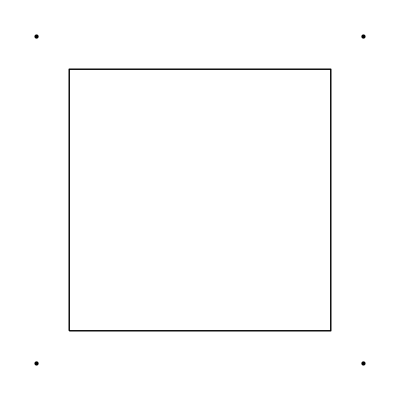

```mathematica
Module[{verts,polys},
verts={{0,0},{1,0},{1,1},{0,1}};
polys={{1,2,3,4}};
Graphics[{Point/@verts,PolyLines[verts,polys]}]]
```

### Generic 2D graph rendering

#### GenericGraphGraphics[verts, edges, faces, opts] (options) VertexLabels, EdgeLabels, FaceLabels, DirectedEdges, VertexColor, EdgeColor, FaceColor, FaceColoring, Options[Graphics]

GenericGraphGraphics[verts, edges, faces, opts] takes lists of 2D vertices, edges, and (optionally) faces, and displays them as a graph with labels as a Graphics object. The faces, if present, are outlined with inset polygons.

Arguments:
	verts — a list of 2D vertices.
	edges — a list of index pairs into verts.
	faces — a list of index sets specifying the faces in CCW order.

Options:
	VertexLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith vertex.
	EdgeLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith edge.
	FaceLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith face.
	DirectedEdges → True | False, specifies whether to show direction arrows on the edges
	Faces → True | False, specifies whether to display faces. (If there are no faces, this setting doesn’t matter.)
	VertexColor → color | colors, specifies the base color to use for vertices and their labels.
	EdgeColor → color | colors, specifies the base color to use for edges and their labels.
	FaceColor → color | colors, specifies the base color to use for faces and their labels.
	FaceColoring→None | {f_1, ...}, where each f_i can be -1, 0, or +1 and specifies that the ith face should be colored light, medium, or dark.
	Options[Graphics] are passed through to Graphics.

Returns: a Graphics object containing the desired representation.

Note that VertexLabels and EdgeLabels are symbols that are already defined as options to Graph, but the format of the specification is different for this function. For GenericGraphGraphics, each specification is a list of the graphical objects that represent the labels in the same order as the object that they label and each label includes its position information.

This function is useful for doing a quick visualization of a graph and checking whether it is well-formed; overlapping vertex or edge labels imply duplicate vertices; improperly drawn faces imply improper parsing into face lists.

GenericGraphGraphics actually works if we pass 3D vertices and you change the wrapper from Graphics to Graphics3D. We use this in the definition of GenericGraphGraphics3D, below.

```mathematica
FaceLabels::usage="FaceLabels is an option to GenericGraphGraphics that specifies labels on the faces of a graph.";
```

```mathematica
DirectedEdges::usage="DirectedEdges is an option to GenericGraphGraphics that displays arrows on the edges of a graph.";
```

```mathematica
VertexColor::usage="VertexColor is an option to GenericGraphGraphics that specifies the color or colors to use for vertices and their labels.";
```

```mathematica
EdgeColor::usage="EdgeColor is an option to GenericGraphGraphics that specifies the color or colors to use for edges and their labels.";
```

```mathematica
FaceColor::usage="FaceColor is an option to GenericGraphGraphics that specifies the color or colors to use for faces and their labels.";
```

```mathematica
FaceColoring::usage = "FaceColoring is an option to GenericGraphGraphics that colors the faces depending on whether each entry in the list is +1 or -1.";
```

```mathematica
Options[GenericGraphGraphics]={
VertexLabels->Automatic,
EdgeLabels->Automatic,
FaceLabels->Automatic,
DirectedEdges->False,
VertexColor->DarkGray,
EdgeColor->Red,
FaceColor->Green,
FaceColoring->None
};
```

```mathematica
GenericGraphGraphics[verts_List,edges_List,faces_:{},opts___]:=Module[{vl,el,fl,de,vc,ec,fc,fcng,hf,gg},
vl=VertexLabels/.{opts}/.Options[GenericGraphGraphics];
el=EdgeLabels/.{opts}/.Options[GenericGraphGraphics];
fl=FaceLabels/.{opts}/.Options[GenericGraphGraphics];
de=DirectedEdges/.{opts}/.Options[GenericGraphGraphics];
vc=VertexColor/.{opts}/.Options[GenericGraphGraphics];
ec=EdgeColor/.{opts}/.Options[GenericGraphGraphics];
fc=FaceColor/.{opts}/.Options[GenericGraphGraphics];
fcng=FaceColoring/.{opts}/.Options[GenericGraphGraphics];
hf = !(faces === {});
If[!ListQ[vc],vc=Table[vc,{Length[verts]}]];
If[!ListQ[ec],ec=Table[ec,{Length[edges]}]];
If[!ListQ[fc],fc=Table[fc,{Length[faces]}]];
gg = {};
If[hf,
If[!(fcng===None),
AppendTo[gg,MapThread[Style[Polygon[verts⟦#1⟧],Lighter[fc,.9-.05#2]]&,{faces,fcng}]]];
AppendTo[gg,MapThread[Style,{PolyLines[verts,faces],fc}]]];
AppendTo[gg,MapThread[Style[#1,#2]&,{If[de,DirectedEdgeLines,EdgeLines][verts,edges],ec}]];
If[hf&&!(fl===None),
AppendTo[gg,MapThread[Style,{If[fl===Automatic,StdFaceLabels[verts,faces],fl],Darker/@fc}]]];
If[!(el===None),
AppendTo[gg,MapThread[Style,{If[el===Automatic,StdEdgeLabels[verts,edges],el],Darker/@ec}]]];
If[!(vl===None),AppendTo[gg,MapThread[Style,{If[vl===Automatic,StdVertexLabels[verts],vl],Darker/@vc,Table[AbsolutePointSize[4],{Length[verts]}]}]]];
Graphics[gg,FilterRules[{opts},Options[Graphics]]]]
```

Example, no face data. This also shows how Graphics options are passed through to Graphics.

```mathematica
Module[{verts,edges},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
GenericGraphGraphics[verts,edges,{},DirectedEdges->True,PlotLabel->"GenericGraphGraphics"]
]//ShowExample
```

Example with colored faces, no edge labels, and individually colored edges.

```mathematica
Module[{verts,edges,faces,ec,fc},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
faces={{1,2,3},{3,4,1}};
ec={Magenta,Brown,Orange,Gray,Purple};
fc={-1,+1};
GenericGraphGraphics[verts,edges,faces,FaceColoring->fc,EdgeLabels->None,EdgeColor->ec]
]//ShowExample
```

### Generic 3D graph rendering

#### GenericGraphGraphics3D[verts, edges, faces, opts] (options) VertexLabels, EdgeLabels, FaceLabels, DirectedEdges, VertexColor, EdgeColor, FaceColor, FaceColoring, Options[Graphics3D]

GenericGraphGraphics3D[verts, edges, faces, opts] takes lists of 3D vertices, edges, and (optionally) faces, and displays them as a graph with labels as a Graphics3D object. The faces, if present, are outlined with inset polygons.

```mathematica
GenericGraphGraphics3D[verts_List,edges_List,faces_:{},opts___]:=Graphics3D@@GenericGraphGraphics[verts,edges,faces,opts]
```

Example

Example, no face data. This also shows how Graphics options are passed through to Graphics.

```mathematica
Module[{verts,edges},
verts={{0,0,0},{1,0,0},{1,.5,0},{0,.5,0}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
GenericGraphGraphics3D[verts,edges,{},DirectedEdges->True,PlotLabel->"GenericGraphGraphics3D"]
]//ShowExample
```

Example with colored faces, no edge labels, and a different edge color.

```mathematica
Module[{verts,edges,faces,fc},
verts={{0,0,0},{1,0,0},{1,.5,0},{0,.5,0}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
faces={{1,2,3},{3,4,1}};
fc={-1,+1};
GenericGraphGraphics3D[verts,edges,faces,FaceColoring->fc,EdgeLabels->None,EdgeColor->Blue]
]//ShowExample
```

## Tessellatica objects

#### Notes

Once we start working with plane graphs and more complicated structures, we will be manipulating collections of data that we will refer to as a Tessellatica object, or TObj. The structure of a TObj is:
	TObj[{property_1→value_1, property_2→value_2, ...}]
A TObj provides a way to encapsulate a bunch of related data in a single object. Instead of having to pass a bunch of lists to a function (like {verts, edges, faces...}), you can pass a TObj that includes the properties Vertices, Edges, and Faces. We include functions for easy extraction of properties and also for error-checking to insure that required properties are present when passing a TObj to a function.

Functions can add data to the TObj by adding new properties and can alter TObj’s by changing existing properties. This section provides a set of functions for creating and working with TObj’s.

### Class TObj

#### Class TObj

TObj is the Head of all Tessellatica objects.

```mathematica
TObj::usage="TObj is the Head of all Tessellatica objects.";
```

#### GetAllRules[tobj] GetAllProperties[tobj]

GetAllRules[tobj] converts tobj to a regular list of rules. Normally, you should use GetValue and GetValues (see below) to access a TObj’s property, but GetAllRules is a handy way to see the entire contents of a TObj. We also use it in some legacy examples where Tessellatica 1 used lists of rules.

```mathematica
GetAllRules[TObj[args_List]]:=args;
```

Example

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2}];
GetAllRules[tobj]
]//ShowExample
```

GetAllProperties[tobj] returns a list of all of the properties in tobj.

```mathematica
GetAllProperties[TObj[args_List]]:=First/@args
```

Example

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->4}];
GetAllProperties[tobj]
]//ShowExample
```

#### Chaining

Most functions that alter a TObj exist in two forms: DoSomethingTo[tobj, parms], and DoSomething[parms]. The latter is a pure function and is provided because it supports a programming idiom common in object-oriented systems, of chaining object methods, using Mathematica’s postfix “//” operator. It allows statements of the form
	tobj = tobj // DoSomething // DoSomethingElse // DoStilAnotherThing[parms] ...
and so forth to successively build up and/or modify an object. You will see many examples of this is the examples for each function.

#### ReplacePropertyIn[tobj, rule] ReplaceProperty[rule] ReplacePropertiesIn[tobj, rules] ReplaceProperties[rules] AddPropertyTo[tobj, rule] AddProperty[rule] AddPropertiesTo[tobj, rules] AddProperties[rules]

ReplacePropertyIn[tobj, rule] replaces a single property in tobj with the corresponding one in rule and returns the result. If tobj doesn’t contain the property, rule is ignored.

```mathematica
ReplacePropertyIn[tobj_TObj,rule_Rule]:=Module[{pos},
pos=Flatten[Position[tobj⟦1⟧,First[rule]->_,1]];
If[Length[pos]≠0,TObj[ReplacePart[tobj⟦1⟧,pos⟦1⟧->rule]],tobj]
]
```

Example.

```mathematica
Module[{tobj,tobj1},
tobj=TObj[{A->1,B->2,C->3}];
tobj1=ReplacePropertyIn[tobj,A->4];
GetAllRules[tobj1]
]//ShowExample
```

Example. This shows that if one property is itself a TObj, the inner TObj is left unaffected.

```mathematica
Module[{tobj,tobj1},
tobj=TObj[{A->1,B->2,C->3,D->TObj[{A->1}]}];
tobj1=ReplacePropertyIn[tobj,A->4];
InputForm[tobj1]
]//ShowExample
```

ReplaceProperty[rule] returns a pure function that replaces the property in its argument with rule.

```mathematica
ReplaceProperty[rule_Rule]:=ReplacePropertyIn[#,rule]&
```

ReplacePropertiesIn[tobj, rules] replaces any properties in tobj with the corresponding ones in rules. If tobj doesn’t contain one of the replacement rules, the rule is ignored.

```mathematica
ReplacePropertiesIn[tobj_TObj,rules_List]:= Module[{tobj1},
tobj1=tobj;
(tobj1=ReplacePropertyIn[tobj1,#])&/@rules;
tobj1]
```

```mathematica
Module[{tobj,tobj1},
tobj=TObj[{A->1,B->2,C->3}];
tobj1=ReplacePropertiesIn[tobj,{C->4,D->5}];
GetAllRules[tobj1]
]//ShowExample
```

ReplaceProperties[rules] returns a pure function that replaces the properties in its argument with rules.

```mathematica
ReplaceProperties[rules_List]:=ReplacePropertiesIn[#,rules]&
```

AddPropertyTo[tobj, rule] adds the specified properties to tobj, replacing any preexisting property of the same name or adding a new one if it didn’t exist, and returning the modified TObj.

```mathematica
AddPropertyTo[tobj_TObj, rule_Rule]:=If[MemberQ[GetAllProperties[tobj],First[rule]],ReplacePropertyIn[tobj,rule],
TObj[Append[GetAllRules[tobj],rule]]]
```

Example. Property already exists.

```mathematica
Module[{tobj,tobj1},
tobj=TObj[{A->1,B->2,C->3}];
tobj1=AddPropertyTo[tobj,C->4];
GetAllRules[tobj1]
]//ShowExample
```

Example. Property does not exist.

```mathematica
Module[{tobj,tobj1},
tobj=TObj[{A->1,B->2,C->3}];
tobj1=AddPropertyTo[tobj,D->5];
GetAllRules[tobj1]
]//ShowExample
```

AddProperty[rule] returns a pure function that adds the property rule to its argument.

```mathematica
AddProperty[rule_Rule]:=AddPropertyTo[#,rule]&
```

AddPropertiesTo[tobj, rules] adds the specified properties to tobj, replacing any preexisting properties of the same value.

```mathematica
AddPropertiesTo[tobj_TObj, rules_List]:=Module[{tobj1},
tobj1=tobj;
(tobj1 = AddPropertyTo[tobj1,#])&/@rules;
tobj1]
```

Example. Some exist, some don’t.

```mathematica
Module[{tobj,tobj1},
tobj=TObj[{A->1,B->2,C->3}];
tobj1=AddPropertiesTo[tobj,{B->4,D->5,E->6}];
GetAllRules[tobj1]
]//ShowExample
```

AddProperties[rules] returns a pure function that adds the properties in rules to its argument.

```mathematica
AddProperties[rules_List]:=AddPropertiesTo[#,rules]&
```

#### HasPropertyQ[tobj, property] AssertProperty[tobj, property] AssertProperties[tobj, properties]

HasPropertyQ[tobj, property] returns True if tobj contains the given property and False otherwise.

```mathematica
HasPropertyQ[tobj_TObj, property_Symbol]:=MemberQ[GetAllProperties[tobj],property]
```

Example

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2}];
Print["HasPropertyQ[tobj,A]: ",HasPropertyQ[tobj,A]];
Print["HasPropertyQ[tobj,C]: ",HasPropertyQ[tobj,C]];
GetAllRules[tobj]
]//ShowExample
```

AssertProperty[tobj, property] checks whether tobj contains property. If not, issue an error message and Abort[]. You will normally not use this; instead, you should use AssertClass (see below) when possible.

```mathematica
AssertProperty::missing = "`1` is missing required property `2`.";
```

```mathematica
AssertProperty[tobj_TObj, property_Symbol]:=If[!MemberQ[GetAllProperties[tobj],property],Message[AssertProperty::missing,tobj,property];Abort[]]
```

Example: property is present.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2}];
AssertProperty[tobj,A]
]//ShowExample
```

Example: a missing property.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2}];
AssertProperty[tobj,C]
]//ShowErrorExample
```

AssertProperties[tobj, properties] checks whether tobj contains every property in the list properties (it may have additional ones). If not, issue an error message and Abort[].

```mathematica
AssertProperties::missing="`1` is missing required properties `2`.";
```

```mathematica
AssertProperties[tobj_TObj, properties_List]:=Module[{missing},
missing=Complement[properties,GetAllProperties[tobj]];
If[!ListEmptyQ[missing],Message[AssertProperties::missing,tobj,missing];Abort[]]]
```

Example: all properties present.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2}];
AssertProperties[tobj,{A,B}]]//ShowExample
```

Example: a missing property.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2}];
AssertProperties[tobj,{A,B,C,D}]]//ShowErrorExample
```

#### GetValue[tobj, property, opts] GetValues[tobj, properties, opts] GetValues[tobj, All]

GetValue[tobj, property, opts] returns the value of the specified property. Default behavior checks for existence and throws an error if the property is missing, but you can override this by supplying the option CheckProperty→False, in which case if the property is missing, its name is returned.

```mathematica
Options[GetValue]={
AssertProperty->True
};
```

```mathematica
GetValue[tobj_TObj,property_Symbol,opts___]:=Module[{cp},
cp=AssertProperty/.{opts}/.Options[GetValue];
If[cp,AssertProperty[tobj,property]];
property/.GetAllRules[tobj]]
```

Example: property present.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
GetValue[tobj,A]
]//ShowExample
```

Example: missing property.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
GetValue[tobj,D]
]//ShowErrorExample
```

Example: missing property, don’t abort.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
GetValue[tobj,D,AssertProperty->False]
]//ShowExample
```

GetValues[tobj, properties, opts] returns a list of the values of the specified properties in the same order as the properties. It’s an easy way to extract a set of multiple properties from a TObj. Default behavior checks for existence and throws an error if one is missing, but you can override this by supplying the option CheckProperties→False, e.g., if some of the properties are optional.

```mathematica
Options[GetValues]={
AssertProperties->True
};
```

```mathematica
GetValues[tobj_TObj, properties_List,opts___]:=Module[{cp},
cp=AssertProperties/.{opts}/.Options[GetValues];
If[cp,AssertProperties[tobj,properties]];
#/.GetAllRules[tobj]&/@properties
]
```

Example: properties present.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
GetValues[tobj,{B, C}]
]//ShowExample
```

Example: missing properties.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
GetValues[tobj,{B, C,D}]
]//ShowErrorExample
```

Example: missing properties, don’t abort.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
GetValues[tobj,{B, C,D},AssertProperties->False]
]//ShowExample
```

GetAllValues[tobj] returns a list of all of the values of the properties in tobj.

```mathematica
GetAllValues[TObj[args_List]]:=Last/@args
```

Example

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
GetAllValues[tobj]
]//ShowExample
```

#### TObj[...][property] TObj[...][properties]

As an object-oriented shorthand for GetValue, you can call a property from a TObj to get its value.

```mathematica
TObj[args_List][property_Symbol]:=GetValue[TObj[args],property]
```

Example: property present.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
tobj[A]
]//ShowExample
```

Example: missing property.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
tobj[D]
]//ShowErrorExample
```

In the same way, you can call a list of properties from a TObj to get all their values as a list.

```mathematica
TObj[args_List][properties_List]:=GetValues[TObj[args],properties]
```

Example: properties present.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
tobj[{B, C}]
]//ShowExample
```

Example: missing properties.

```mathematica
Module[{tobj},
tobj=TObj[{A->1,B->2,C->3}];
tobj[{B, C,D}]
]//ShowErrorExample
```

#### TClasses MakeTObj[] MakeTObj[class, properties] AddClassTo[tobj, class] AddClassTo[tobj, class, properties] AddClass[class] AddClass[class, properties] HasClassQ[tobj, class] AssertClass[tobj, class, where] AssertClasses[tobj, classes, where]

TClasses is a TObj property that is a list of all object classes that the TObj belongs to. Every TObj has this property. We use it to implement the inheritance hierarchy for TObj’s.

As a shorthand bit of documentation, we will talk about TObj objects as objects by their class. So, for example, we may talk about a TGraph, but really it’s a TObj whose TClasses property contains the symbol TGraph. Since the TClasses property is a list, a TObj can simultaneously be more than one class of TObj by containing multiple entries in this list. This supports an inheritance hierarchy where we can have mixin classes that can join at multiple places in the inheritance hierarchy. The order of the TClasses list in an object typically reflects the order in which the object was built, but you should not use or rely upon this order. In fact, you should never access the TClasses property directly, but instead, should use the getter/setter functions in this section.

```mathematica
TClasses::usage="TClasses is a TObj property that specifies the classes of TObj that a particular TObj belongs to.";
```

MakeTObj creates a new blank TObj. You should always use MakeTObj to create a new TObj; in fact, you should never use the head TObj at all, except to pattern-match in arguments (e.g., MyFunction[tobj_TObj]).

```mathematica
MakeTObj[]:=TObj[{TClasses->{}}]
```

MakeTObj[class, properties] creates a TObj of the specified class and properties.

```mathematica
MakeTObj[class_Symbol,properties_List]:=TObj[Prepend[properties,TClasses->{class}]]
```

AddClassTo[tobj, class] adds the specified class to tobj’s list of classes, i.e., its TClasses property, without altering its other properties.

AddClassTo[tobj, class, properties] adds the specified class and the specified properties as well. This is a useful way to add a mixin class.

```mathematica
AddClassTo[tobj_TObj,class_Symbol,properties_List:{}]:=AddPropertiesTo[tobj,Prepend[properties,TClasses->Append[GetValue[tobj,TClasses],class]]]
```

Example: just the class.

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}];
tobj=AddClassTo[tobj,Y];
GetAllRules[tobj]
]//ShowExample
```

Example: class and new properties.

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}];
tobj=AddClassTo[tobj,Y,{C->3}];
GetAllRules[tobj]
]//ShowExample
```

AddClass[class] returns a pure function that adds the specified class to its argument.

AddClass[class, properties] returns a pure function that adds the specified class and properties to its argument.

```mathematica
AddClass[class_Symbol,properties_List:{}]:=AddClassTo[#,class,properties]&
```

Example: just the class

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}] // AddClass[Y];
GetAllRules[tobj]
]//ShowExample
```

Example: class and new properties.

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}]//AddClass[Y,{C->3}];
GetAllRules[tobj]
]//ShowExample
```

Example of chaining multiple classes.

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}]//AddClass[Y,{C->3}]//AddClass[Z,{D->4}];
GetAllRules[tobj]
]//ShowExample
```

HasClassQ[tobj, class] returns True if tobj belongs to TClasses class. A class is different from a property because a TObj can only have a single value for each property but it can belong to several classes at the same time. Typically classes will be related to one another in an inheritance hierarchy.

```mathematica
HasClassQ[tobj_TObj, class_Symbol]:=MemberQ[GetValue[tobj,TClasses],class]
```

AssertClass[tobj, class, where] returns True if the TObj belongs to the given class. If it doesn’t, it  issues an error message and Aborts using where to describe the context, typically, the name of the calling function or definition.

AssertClass helps you deal with the common Mathematica phenomenon that an error occurs deeply inside a nested series of functions and Mathematica barfs, but continues on its merry way, spewing errors galore to the Messages console until it finally encounters a fatal error. In our system, we assume that all dynamic type errors are fatal. Iif you’ve made a type error (passing the wrong kind of class to a function), you don’t want Mathematica to keep trying things with the deficient object; you want it to stop right there and flag the error. So, most publicly exposed functions that take TObj’s as arguments check the class(es) of the passed-in arguments and if they aren’t of the right type, it aborts and tells you at least what function the error happened inside of.

```mathematica
AssertClass::missing="In `1`, `2` is not a `3`.";
```

```mathematica
AssertClass::nottobj="`1` is not a TObj.";
```

```mathematica
AssertClass[tobj_,___]:=(Message[AssertClass::nottobj,tobj];Abort[];)
```

```mathematica
AssertClass[tobj_TObj, class_Symbol,where_:"<unspecified>"]:=If[MemberQ[GetValue[tobj,TClasses],class],True,
Message[AssertClass::missing,where,tobj,class];Abort[]]
```

Example: success

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}];
AssertClass[tobj,X]
]//ShowExample
```

Example: fail, not a TObj

```mathematica
Module[{tobj},
tobj="Not A Tobj";
AssertClass[tobj,Y]
]//ShowErrorExample
```

Example: fail, wrong class

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}];
AssertClass[tobj,Y]
]//ShowErrorExample
```

Example: fail, with context

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}];
AssertClass[tobj,Y,"EXAMPLE"]
]//ShowErrorExample
```

AssertClasses[tobj, classes, where] returns True if the TObj belongs to all of the specified classes. If it doesn’t, it issues an error message on the first failure and aborts.

```mathematica
AssertClasses::nottobj="`1` is not a TObj.";
```

```mathematica
AssertClasses[tobj_,___]:=(Message[AssertClasses::nottobj,tobj];Abort[];)
```

```mathematica
AssertClasses[tobj_TObj,classes_List,where_:"<unspecified>"]:=And@@(AssertClass[tobj,#,where]&/@classes)
```

Example: success

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}];
AssertClasses[tobj,{X}]
]//ShowExample
```

Example: fail, with context

```mathematica
Module[{tobj},
tobj=MakeTObj[X,{A->1,B->2}];
AssertClasses[tobj,{X,Y,Z},"EXAMPLE"]
]//ShowErrorExample
```

#### Format[tobj]

The  display format of a TObj shows a list of its classes.

```mathematica
Format[TObj[args_List]]^:=Module[{classes},
classes=TClasses/.args;
If[classes==TClasses,classes={}];
"⁃TObj:<"<>StringJoin[Riffle[ToString/@classes,", "]]<>">⁃"]
```

Example

```mathematica
Module[{tobj},
tobj=TObj[{TClasses->{A, B},C->1,D->2}];
tobj]//ShowExample
```

Example: class missing.

```mathematica
Module[{tobj},
tobj=TObj[{C->1,D->2}];
tobj]//ShowExample
```

#### Class structure <class> Add<class>To[tobj, parms_i, ...] Add<class>[parms_i, ...] Make<class>[parms_i, ...]

When I create a new TObj class, I  define a symbol for its class name (via <class>::usage) and then define any new properties introduced in the class.

A base class is built directly from one or more parameters. The most common base class in Tessellatica is class TGraph.

A derived class is a class that must inherit from another class, which could be a base class or another derived class. An example of a derived class is class TPlaneGraph, which must inherit from a TGraph.

A mixin class is a class that can be a base class but is commonly used to add behaviors and properties to another class, via multiple inheritance. An example of a mixin class is the TAssigned class, which is used to add crease assignment to the TGraph class (and its subclasses).

A multiple-inheritance class is a conceptual class (with no actual names or functions) that we use to describe an object that inherits from two or more classes via different parentage. A general way of referring to the class structure of a multiple-inheritance class is to combine the class names with a “+“ sign; thus, an object that inherits from both TGraph and TAssigned would have a TGraph+TAssigned class. This usage is only for purposes of documentation and discussion; there’s no actual class name called “TGraph+TAssigned,” for example. But for a few common combinations, we do define classes, see next.

A convenience class is a class defined by multiple inheritance. An example of a convenience class is the TGraphAssigned class, which inherits from both TGraph and TAssigned classes. The number of ways you can combine base classes, derived classes, and mixin classes is quite large; we create convenience classes only for the most common combinations.

Convenience classes are more specific than multiple-inheritance classes, which makes them of lesser stature. So, for example, while an TGraphAssigned class is a TGraph+TAssigned class, and a TPlaneGraphAssigned is also a TGraph+TAssigned class, a TPlaneGraphAssigned is NOT necessarily a TGraphAssigned, depending on the order of its construction. So, when we do class checking on class arguments using AssertClasses, we never check against a convenience class, but rather, against the relevant parent classes.

Classes can have multiple forms of constructor:
	Add<class>To[tobj, [parms_1, parms_2, ...] takes a base class object and adds the new class to it. The parameter list contains only the additional parameters that are needed for the new class.
	Add<class>[parms_1, parms_2, ...] returns a pure function that acts on a base class object and adds the additional parameters to the base class, returning the new class object.
For some classes we provide a third form:
	Make<class>[parms_1, parms_2, ...] builds the object directly from all required parameters. This form will only be provided if the parameter list is relatively short and the inheritance hierarchy is direct.

Constructors for base classes only provide the Make<class>[parms_1, parms_2, ...] constructor.

Constructors for derived classes only provide the Add<class>To[tobj_TObj, parms_1, parms_2, ...] and Add<class>[parms_1, parms_2, ...] constructors.

Mixin classes provide the Add<class>To[tobj_TObj, parms_1, parms_2, ...] and Add<class>[parms_1, parms_2, ...] constructors but may also provide a Make<class>[parms_1, parms_2, ...] constructor if they can act as a base class.

Several classes take no additional parameters in their Add<class>To constructor; they simply take an argument of one class (e.g., TGraph) and return an argument of the new class (e.g., TPlaneGraph). For these classes, Add<class> and Add<class>To behave exactly the same.

Convenience classes may provide different forms of a Make<class> function, depending on how long and complicated their properties are. Relatively simple ones (e.g., TGraphAssigned) will take the full set of properties as a sequence of parameters. More complex ones (e.g., TPlaneGraphAssigned) will take a base TObj plus one or more parameters, similar to Add<class>To.

The Add<class>To and Add<class> constructors allow you to build up derived classes by chaining constructors for base and mixin classes using Mathematica’s postfix “//” operator. For example:
	MakeTGraph[verts, edges] // AddTPlaneGraph // AddTGraphAssigned[types]
This expression returns a TPlaneGraph+TGraphAssigned, i.e., a plane graph with adjacency information and crease assignments on its edges.

Functions that take TObjs as arguments have some notations under their names in the subsubsection titles:
	(unchecked class) ... means that the TObj should be of the specified class but there is no explicit class-checking.
	(checked class) ... means that the TObj should have the specified class(es) and if it doesn’t, an error will be thrown that aborts the function.
Typically we use “unchecked class” for helper functions and use “checked class” for functions intended for general usage. Helper functions are, roughly speaking, equivalent to private methods in OO lingo. Mathematica supports true private functions via namespaces, but in Tessellatica we expose all functions, which facilitates ongoing development of the package.

#### Class hierarchy $TClasses $TClassInheritance RegisterTClass[class, parents] TClassGraphics[opts] (options) ClassGraphRotation, FontSize

$TClasses is a list of all of the TObj classes that have been defined.

```mathematica
$TClasses={};
```

$TClassInheritance is a list of the edges of the $TObj classes graph as index pairs into $TClasses.

```mathematica
$TClassInheritance={};
```

RegisterTClass[class, parents] registers TClasses class in the TObj class hierarchy. If it is a child class, provide a list of its parents in parents.

Call RegisterTClass for every class that’s created.

```mathematica
RegisterTClass[class_Symbol,parents_List:{}]:=Module[{ci,ce},
If[MemberQ[$TClasses,class],Return[]];(* don't if we've already registered *)
AppendTo[$TClasses,class];
ci=Length[$TClasses];
(ce=Position[$TClasses,#]⟦1,1⟧->ci;If[!MemberQ[$TClassInheritance,ce],
AppendTo[$TClassInheritance,ce]])&/@parents
]
```

TClassGraphics[opts] returns a Graphics object that displays the TObj class hierarchy. Options are:
	GraphRotation → θ, rotates the graph by an angle θ so that labels don’t overlap one another.
	FontSize → size, specifies the font size for the labels.

```mathematica
ClassGraphRotation::usage="ClassGraphRotation is an option to TClassGraphics that specifies the angle to rotate the class hierarchy graph.";
```

```mathematica
Options[TClassGraphics]={
ClassGraphRotation->-60°,
FontSize->14
};
```

```mathematica
TClassGraphics[opts___]:=Module[{gr,fs,rm,g},
gr=ClassGraphRotation/.{opts}/.Options[TClassGraphics];
fs=FontSize/.{opts}/.Options[TClassGraphics];
rm=RotationMatrix2D[gr];
g=LayeredGraphPlot[$TClassInheritance,Left,VertexRenderingFunction->({Style[Point[#1],AbsolutePointSize[5],DarkGray],Style[Text[$TClasses⟦#2⟧,#1,{-1.1,-1.1}],FontSize->fs]}&)];
g/.
GraphicsComplex[pts_,stuff___]:>GraphicsComplex[rm.#&/@pts,stuff]/.Point[x_]:>Point[rm.x]/.Text[label_,y_,pos_]:>Text[label,rm.y,pos]]
```

See the end of the notebook for an example of TClassGraphics, after all classes have been defined.

#### Tessellatica rendering functions

There are a number of functions that can be used to visualize and/or render different Tessellatica objects. They are defined further down, but for convenience, we summarize them here.

GenericGraphGraphics[verts, edges, faces, opts] -- This is not a Tessellatica object renderer, but is a useful tool for basic rendering of plane graphs.

--Functions that render Tessellatica objects--

GraphGraphics[tobj, opts] takes a TGraph, displays vertices, edges, and faces, with numbers and labels.

Graph2DGraphics[tobj, opts] takes a TGraph2D and displays the graph using the alternate embedding Vertices2D.

FoldAngleGraphics[tobj, opts] takes a TGraph3D and displays the graph with the original embedding but the edges labeled by its FoldAngles.

Graph3DGraphics3D[tobj, opts] takes a TGraph3D and displays the graph using the alternate embedding Vertices3D.

PrimalDualGraphics[tobj, opts] takes a TPrimalDualGraph and displays both the primal and dual graph, overlaid or side-by-side.

--Functions that render with symbolic styles--

CreasePatternGraphics[tobj, opts] takes a TGraph+TAssigned and returns a rendering of the crease pattern.

GenericFoldedFormGraphics[tobj, opts] takes a TGraph2D+TAssigned and returns a generic rendering of the 2D folded form.

VisibleFoldedFormGraphics[tobj, opts] takes a TGraph2D+TAssigned and returns a rendering of the 2D folded form with hidden line removal (not guaranteed to be exact).

GenericPairGraphics[tobj, opts] takes a TGraph2D+TAssigned and returns a side-by-side pair of the crease pattern and folded form to the same scale, using the generic folded form.

VisiblePairGraphics[tobj, opts] takes a TGraph2D+TAssigned and returns a side-by-side pair of the crease pattern and folded form to the same scale, using the visible folded form (with hidden line removal).

FoldAngleCreasePatternGraphics[tobj, opts] takes a TGraph3D+TAssigned and returns a rendering of the crease pattern with fold angles labeled with their numerical values.

FoldedFormGraphics3D[tobj, opts] takes a TGraph3D+TAssigned and returns a rendering of the 3D folded form.

--Renderers for specialized objects--

LFFGraphGraphics[tobj, opts] takes a TLFFGraph and returns a rendering of the local flat foldability conditions it represents.

VertexCreasePatternGraphics[tobj, opts] takes a TVertex and returns a rendering of the vertex crease pattern as a circular disk.

VertexGenericFoldedFormGraphics[tobj, opts] takes a TVertex and returns a generic rendering of the folded form  (no hidden line removal) as a folded circular disk.

Vertex3DCreasePatternGraphics[tobj, opts] takes a TVertex3D and returns a rendering of the crease pattern as a circular disk.

Vertex3DFoldedFormGraphics3D[tobj, opts] takes a TVertex3D and returns a rendering of the 3D folded form as a folded circular disk.

Vertex3DGaussianSphereGraphics3D[tobj, opts] takes a TVertex3D and returns a rendering of the Gaussian sphere.

Vertex3DGraphicsTrio[tobj, opts] takes a TVertex3D and returns a GraphicsRow of all three renderings: crease pattern, folded form, and Gaussian sphere.

Degree4Vertex3DCreasePatternGraphics[tobj, opts] takes a TDegree4Vertex3D and returns a rendering of the crease pattern as a circular disk.

Degree4Vertex3DFoldedFormGraphics3D[tobj, opts] takes a TDegree4Vertex3D and returns a rendering of the 3D folded form as a circular disk, along with additional relevant vectors and planes.

Degree4Vertex3DGaussianSphereGraphics3D[tobj, opts] takes a TDegree4Vertex3D and returns a rendering of the Gaussian sphere, along with additional relevant vectors and planes.

Degree4Vertex3DGraphicsPair[tobj, opts] takes a TDegree4Vertex3D and returns a GraphicsRow of the crease pattern and folded form.

Degree4Vertex3DGraphicsTrio[tobj, opts] takes a TDegree4Vertex3D and returns a GraphicsRow of all three renderings: crease pattern, folded form, and Gaussian sphere.

TwistFoldedFormGraphics[tobj, opts] takes a TGraph2D+TAssigned+TTwistGraph and returns a rendering of the folded form with hidden line removal that makes use of information about the twist to handle overlaps better than VisibleFoldedFormGraphics.

--Lower-level renderers for twists--

These functions do not take TObj arguments.

CircularPolygonTwistCreasePatternGraphics[verts, α, r, types, opts] returns a polygon twist crease pattern, clipped to a circle.

CircularPolygonTwistFoldedFormGraphics[verts, α, r, types, opts] returns a polygon twist folded form, clipped to a circle.

CircularRegularPolygonTwistCreasePatternGraphics[n, α, m, types, opts] returns a unit regular polygon twist crease pattern, clipped to a circle.

CircularRegularPolygonTwistFoldedFormGraphics[n, α, m, types, opts] returns a unit regular polygon twist folded form, clipped to a circle.

CircularRegularPolygonTwistPairGraphics[n, α, m, types, opts] returns a side-by-side rendering of crease pattern and folded form.

CircularTriangleTwistCreasePatternGraphics[angles, α, r, types, opts] returns a triangle twist crease pattern, clipped to a circle.

CircularTriangleTwistFoldedFormGraphics[angles, α, r, types, opts] returns a triangle twist folded form, clipped to a circle.

--Tiling renderers--

There are a host of rendering functions in the section “Tiling-based tessellations.” Since they are quite specialized, won’t include them here.

## Tessellatica graphs

#### Notes

A planar graph is one that can be drawn in the plane with no crossing edges. A plane graph is a planar graph together with a non-crossing embedding. This section contains functions for manipulating and drawing planar and plane graphs, which, for obvious reasons, are highly relevant in origami design, since crease patterns are all plane graphs and flat folded forms are all planar graphs. This section makes use of two Mathematica packages: the ComputationalGeometry package and the Combinatorica package. The latter contains functions for manipulating graphs and has its own native representation for graphs—which we don’t use (most of the time). We will represent graphs by lists of vertices, edges, and other properties that are particular to plane graphs: faces, vertex adjacency lists, and the like, as well as decorations of both the edges and faces with crease type, face coloring, and so forth.

This is the first place we introduce TObj (Tessellatica object) to represent complex objects with multiple related properties. We introduce the first class, TGraph, and the first properties: Vertices, Edges, and Faces. Additional properties will be introduced as their need arises.

As a general rule, functions that take only a single list and/or low-level functions used internally will take lists and/or parameters as arguments and will return TObj’s. Functions whose input requires two or more related lists will generally take TObj’s as arguments. If an input list is “consumed in processing” (like bverts in CircularlyAddEdges), it will be passed as an additional function argument, rather than as a TObj property.

### Class TGraph

#### TObj class: TGraph Inherits from: none

TGraph is a TObj class that represents a graph, containing {Vertices, Edges, Faces} properties. It represents a general graph object using our own preferred representation. Faces can be empty.

```mathematica
TGraph::usage="TGraph s a TObj class that represents a graph.";
```

I’d really like to make this just plain Graph, but Combinatorica had already adopted that symbol for its own nefarious purposes. And then Mathematica 11 introduced a native Graph symbol, so it was probably just as well.

```mathematica
RegisterTClass[TGraph];
```

#### TGraph properties: Vertices Edges Faces

Vertices→{v_1,v_2, ...} is a TObj property that specifies the list of vertices in a plane graph, where each of the v_i is a 2D point.

```mathematica
Vertices::usage = "Vertices is a TObj property that specifies a list of vertex coordinates.";
```

Edges→{{v_(1,a,)v_(1,b)}, {v_(2,a), v_(2,b)}, ...} is a TObj property that specifies a set of directed or undirected edges in a plane graph as a list of vertex index pairs.

```mathematica
Edges::usage = "Edges is a TObj property that specifies a list of edges as index pairs on a list of vertices.";
```

Faces→{{v_(1,a,)v_(1,b), ...}, {v_(2,a), v_(2,b), ...}, ...} is a TObj property that specifies a list of faces in a plane graph as a list of vertex indices in CCW order around the face.

```mathematica
Faces::usage="Faces is a TObj property that specifies a list of faces, each face being a list of indices on a list of vertex coordinates.";
```

#### AddTGraphTo[tobj, verts, edges] AddTGraphTo[tobj, verts, edges, faces] AddTGraph[verts, edges] AddTGraph[verts, edges, faces] MakeTGraph[verts, edges] MakeTGraph[verts, edges, faces]

AddTGraphTo[tobj, verts, edges, faces] takes a TObj and adds a TGraph to it. faces are optional.

```mathematica
AddTGraphTo[tobj_TObj, verts_List,edges_List,faces_List:{}]:=AddClassTo[TGraph,{Vertices->verts,Edges->edges,Faces->faces}]
```

AddTGraph[verts, edges, faces] returns a pure function that adds a TGraph to its argument.

```mathematica
AddTGraph[verts_List,edges_List,faces_List:{}]:=AddTGraphTo[#,verts,edges,faces]&
```

MakeTGraph[verts, edges, faces] returns a TGraph containing vertices verts, edges edges, and faces faces. faces are optional.

```mathematica
MakeTGraph[verts_List,edges_List,faces_List:{}]:=MakeTObj[TGraph, {Vertices->verts,Edges->edges,Faces->faces}];
```

Note that if you do not supply faces, none will be computed. Use class TPlaneGraph (see next section) to add faces to a TGraph that is lacking them.

#### HasFacesQ[tobj] (unchecked class) TGraph

HasFacesQ[tobj] returns True if the TGraph contains any Faces.

```mathematica
HasFacesQ[tobj_TObj]:=!ListEmptyQ[GetValue[tobj,Faces]]
```

#### Make<qualifiers>Graph[parms_i, ...]

TGraph constructors have a few well-defined naming conventions, as described above for general Tessellatica objects. Make<class> returns an object of type <class>.

Class TGraph has many subclasses and we define various functions that will return instances of one or more subclass. So as to avoid rampant name expansion, we don’t work the full class name of the returned type into the function name. All of these will have the form Make<qualifiers>Graph, where <qualifiers> describes what the return object is. But it won’t include class name qualifiers like Assigned, Plane, 2D, or 3D (unless there’s actually both 2D and 3D flavors of the same thing). So you’ll need to read the function docs to determine what class is specifically returned. Such names will not include the T; you’ll only see that for a specific class’s Make constructor. So:
	MakeTSomethingGraph — is a Make constructor for class TSomethingGraph.
	MakeSomethingElseGraph — is a Make function that returns some subclass of TGraph.

### TGraph rendering

#### GraphGraphics[tobj, opts] (checked class) TGraph (options) Options[GenericGraphGraphics], Options[Graphics]

GraphGraphics[tobj, opts] takes a TGraph and displays vertices, edges, and faces with labels as a Graphics object. The faces, if present, are outlined with inset polygons.

Options:
	Options[GenericGraphGraphics] are passed through to GenericGraphGraphics.
	Options[Graphics] are passed through to Graphics.

This function is useful for doing a quick visualization of a graph and checking whether it is well-formed; overlapping vertex or edge labels imply duplicate vertices; improperly drawn faces imply improper parsing into face lists.

```mathematica
GraphGraphics[tobj_TObj,opts___]:=Module[{vl,el,fl,de,fd,fc,verts, edges, faces,hf,gg},
AssertClass[tobj,TGraph,GraphGraphics];
{verts, edges, faces} = GetValues[tobj,{Vertices, Edges, Faces},AssertProperties->False];
GenericGraphGraphics[verts,edges,faces,opts]]
```

Example, no face data. This also shows how Graphics options are passed through to Graphics.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
tobj=MakeTGraph[verts,edges];
GraphGraphics[tobj,DirectedEdges->True,PlotLabel->"GraphGraphics"]
]//ShowExample
```

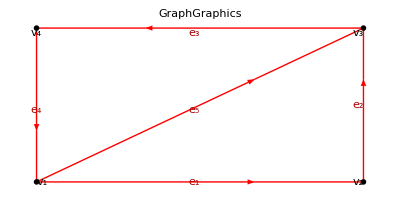

-Graphics-

Example with faces, but no edge labels.

```mathematica
Module[{verts,edges,faces,tobj,fc},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
faces={{1,2,3},{3,4,1}};
fc={-1,+1};
tobj=MakeTGraph[verts,edges,faces];
GraphGraphics[tobj,FaceColoring->fc,EdgeLabels->None]
]//ShowExample
```

### TGraph examples

#### Notes

To illustrate the behavior of various functions, we use a number of simple examples over and over. Rather than reconstructing them from scratch each time we need one, we’ll predefine some examples here, and will continue adding examples throughout.

The general naming scheme will be of the form <description><TGraph type>. For example, everything here is a SomethingGraph (although for the two exceptions that hae no Faces data, that tidbit is appended to the name). Later on, we will have SomethingGraph2D, SomethingGraph3D, SomethingGraph3DAssigned, etc., so that the name tells you something about what type of TGraph it is.

The global variable $TGraphExamples (see next) contains a list of the names of all predefined named examples.

The function ShowTGraphExample (defined at the very end of this package) creates a rendering of any named example, with what, precisely, is rendered depending on the class(es) of the TGraph: whether it’s flat, 2D, or 3D, and/or whether it has a crease assignment.

#### $TGraphExamples

$TGraphExamples is a global list of all examples by name. This list will be incrementally built up over the course of this package.

```mathematica
$TGraphExamples={};
```

#### AddTGraphExample[name, tobj]

AddTGraphExample[name, tobj] records the name as a string in our global list and then assigns the given object to that name. If it is already present, it gets moved to the end of the current list.

```mathematica
AddTGraphExample::badobj="`1` is not a TObj.";
```

```mathematica
AddTGraphExample[name_Symbol,tobj_TObj]:=Module[{namestr},
namestr=ToString[name];
$TGraphExamples=DeleteItems[$TGraphExamples,{namestr}];
AppendTo[$TGraphExamples,namestr];
name=tobj]
```

```mathematica
AddTGraphExample[name_Symbol,any_]:=Module[{},
Message[AddTGraphExample::badobj,any];
Abort[]]
```

#### CrossedSquareGraphNoFaces

CrossedSquareGraphNoFaces is a TGraph of a square with four lines that divide it into four smaller squares. No faces.

```mathematica
Clear[CrossedSquareGraphNoFaces];
AddTGraphExample[CrossedSquareGraphNoFaces,Module[{verts,edges},
verts={{0,0},{2,0},{4,0},{0,2},{2,2},{4,2},{0,4},{2,4},{4,4}};
edges={{2,5},{4,5},{5,6},{5,8},{1,2},{2,3},{3,6},{6,9},{9,8},{8,7},{7,4},{4,1}};
MakeTGraph[verts,edges]]];
```

Example

```mathematica
Module[{tobj},
tobj=CrossedSquareGraphNoFaces;
GraphGraphics[tobj]
]//ShowExample
```

#### CrossedSquareGraph

CrossedSquareGraph is a TGraph of a square with four lines that divide it into four smaller squares, with faces.

```mathematica
Clear[CrossedSquareGraph];
AddTGraphExample[CrossedSquareGraph,Module[{verts,edges,faces},
verts={{0,0},{1,0},{2,0},{0,1},{1,1},{2,1},{0,2},{1,2},{2,2}};
edges={{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{1,4},{2,5},{3,6},{4,7},{5,8},{6,9}};
faces={{1,2,5,4},{2,3,6,5},{4,5,8,7},{5,6,9,8}};
MakeTGraph[verts,edges,faces]]];
```

Example

```mathematica
Module[{tobj},
tobj=CrossedSquareGraph;
GraphGraphics[tobj]
]//ShowExample
```

#### ThreeFoldSquareGraphNoFaces

ThreeFoldSquareGraphNoFaces is a TGraph of a square with three folds, horizontal, vertical, and diagonal. No faces.

```mathematica
Clear[ThreeFoldSquareGraphNoFaces];
AddTGraphExample[ThreeFoldSquareGraphNoFaces,Module[{verts,edges},
verts={{0,0},{1,0},{3,0},{7/2,0},{0,1},{1,1},{2,1},{7/2,1},{1,2},{0,3},{0,7/2},{1,7/2},{7/2,7/2}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8},{5,10},{6,9},{7,9},{8,13},{9,10},{10,11},{9,12},{11,12},{12,13}};
MakeTGraph[verts,edges]]];
```

Example

```mathematica
Module[{tobj},
tobj=ThreeFoldSquareGraphNoFaces;
GraphGraphics[tobj]
]//ShowExample
```

#### ThreeFoldSquareGraph

ThreeFoldSquareGraphNoFaces is a TGraph of a square with three folds, horizontal, vertical, and diagonal. No faces.

```mathematica
Clear[ThreeFoldSquareGraph];
AddTGraphExample[ThreeFoldSquareGraph,Module[{verts,edges,faces},
verts={{0,0},{1,0},{3,0},{7/2,0},{0,1},{1,1},{2,1},{7/2,1},{1,2},{0,3},{0,7/2},{1,7/2},{7/2,7/2}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8},{5,10},{6,9},{7,9},{8,13},{9,10},{10,11},{9,12},{11,12},{12,13}};
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7},{5,6,9,10},{6,7,9},{7,8,13,12,9},{9,12,11,10}};
MakeTGraph[verts,edges,faces]]];
```

Example

```mathematica
Module[{tobj},
tobj=ThreeFoldSquareGraph;
GraphGraphics[tobj]
]//ShowExample
```

#### SimpleSquareTwistGraph

```mathematica
Clear[SimpleSquareTwistGraph];
AddTGraphExample[SimpleSquareTwistGraph,Module[{verts,edges,faces},
verts={{0,0},{1,0},{1,1},{0,1},{-.4,-1},{-.8,-1},{2,-.4},{2,-.8},{1.4,2},{1.8,2},{-1,1.4},{-1,1.8},{-1,-1},{2,-1},{2,2},{-1,2}};
edges={{1,2},{2,3},{4,3},{1,4},(* interior square *)
{1,5},{4,6},{7,2},{8,1},{3,9},{2,10},{4,11},{3,12},(* pleats *)
{13,6},{6,5},{5,14},{14,8},{8,7},{7,15},{15,10},{10,9},{9,16},{16,12},{12,11},{11,13} (* border *)
};
faces={{1,2,3,4},{4,3,12,11},{1,4,6,5},{1,5,14,8},{7,2,1,8},{3,9,16,12},{2,10,9,3},{4,11,13,6},{7,15,10,2}};
MakeTGraph[verts,edges,faces]]];
```

Example

```mathematica
Module[{tobj},
tobj=SimpleSquareTwistGraph;
GraphGraphics[tobj]
]//ShowExample
```

#### SimpleSplitSquareTwistGraph

```mathematica
Clear[SimpleSplitSquareTwistGraph];
AddTGraphExample[SimpleSplitSquareTwistGraph,Module[{verts,edges,faces},
verts={{0,0},{1,0},{1,1},{0,1},{-.4,-1},{-.8,-1},{2,-.4},{2,-.8},{1.4,2},{1.8,2},{-1,1.4},{-1,1.8},{-1,-1},{2,-1},{2,2},{-1,2}};
edges={{1,2},{2,3},{4,3},{1,4},{1,3},(* interior square *)
{1,5},{4,6},{7,2},{8,1},{3,9},{2,10},{4,11},{3,12},(* pleats *)
{13,6},{6,5},{5,14},{14,8},{8,7},{7,15},{15,10},{10,9},{9,16},{16,12},{12,11},{11,13} (* border *)
};
faces={{1,2,3},{4,3,12,11},{1,4,6,5},{1,3,4},{1,5,14,8},{7,2,1,8},{3,9,16,12},{2,10,9,3},{4,11,13,6},{7,15,10,2}};
MakeTGraph[verts,edges,faces]]];
```

Example

```mathematica
Module[{tobj},
tobj=SimpleSplitSquareTwistGraph;
GraphGraphics[tobj]
]//ShowExample
```

#### SingleVertexGraph

SingleVertexGraph gives a single vertex in a square.

```mathematica
Clear[SingleVertexGraph];
AddTGraphExample[SingleVertexGraph,Module[{verts,edges,faces,tobj},
verts={{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,1/√3},{-1,-1},{-1/√3,-1},{1,-1}}//N;
edges={{1,2},{1,4},{1,6},{1,8},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,2}};
faces={{1,2,3,4},{1,4,5,6},{1,6,7,8},{1,8,9,2}};
MakeTGraph[verts,edges,faces]]]
```

⁃TObj:<TGraph>⁃

Example

```mathematica
Module[{tobj},
tobj=SingleVertexGraph;
GraphGraphics[tobj]
]//ShowExample
```

#### CrossPleatedSquareGraph

A square graph with two pleats, one horizontal, one vertical.

```mathematica
Clear[CrossPleatedSquareGraph];
AddTGraphExample[CrossPleatedSquareGraph,Module[{verts,edges,faces,tobj},
verts=Flatten[Table[{i-1+0.1(-1)^i,j-1+0.1(-1)^j},{j,4},{i,4}],1];
edges=Join[Flatten[Table[{i+4(j-1),i+1+4(j-1)},{j,4},{i,3}],1],Flatten[Table[{i+4(j-1),i+4(j)},{j,3},{i,4}],1]];
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7},{5,6,10,9},{6,7,11,10},{7,8,12,11},{9,10,14,13},{10,11,15,14},{11,12,16,15}};
MakeTGraph[verts,edges,faces]]]
```

⁃TObj:<TGraph>⁃

Example

```mathematica
Module[{tobj},
tobj=CrossPleatedSquareGraph;
GraphGraphics[tobj]
]//ShowExample
```

### TGraph index utilities

#### SamePtQ[p1, p2, opts] [deprecated] (options) SamePtTolerance [deprecated] SameEdgeQ[e1, e2] SameFaceQ[f1, f2]

SamePtQ[p1, p2, opts] returns true if the two points lie within a specified tolerance of each other.
Options are:
	SamePtTolerance → tol, where tol is the separation distance below which the two points are considered the same.

2017-06-17. Redefine SamePtQ and SamePtTolerance to make use of the more general functions PtOnPtQ and PtOnLineQ and their associated tolerances. You can still use SamePtQ, but it’s no longer the preferred calling form.

```mathematica
SamePtQ=PtOnPtQ;
SamePtTolerance=PtOnPtTolerance;
```

SameEdgeQ[e1, e2] returns true if the two edges, which are given as index pairs, are equal in either order.

```mathematica
SameEdgeQ=#1==#2||#1==Reverse[#2]&;
```

Examples

```mathematica
SameEdgeQ[{1,2},{2,1}]//ShowExample
```

```mathematica
SameEdgeQ[{1,2},{2,3}]//ShowExample
```

SameFaceQ[f1, f2] returns True if the two faces f1 and f2 are the same, where f1 and f2 are lists of vertex indices, and the test for same-ness is that one is a cylic permutation of the other.

```mathematica
SameFaceQ[f1_,f2_]:=Or@@(f1==#&/@Table[RotateLeft[f2,i],{i,Length[f2]}])
```

Examples

```mathematica
SameFaceQ[{1,2,3},{2,3,1}]//ShowExample
```

```mathematica
SameFaceQ[{1,2,3},{2,3,4}]//ShowExample
```

#### VertexIndex[tobj, v, opts] (options) SamePtTolerance EdgeIndex[tobj, e] FaceIndex[tobj, f]

VertexIndex[tobj, v, opts] returns the index of vertex v within tobj. If it is not found, it returns 0. Options are:
	SamePtTolerance → tol, to specify the tolerance on sameness.

VertexIndex and EdgeIndex have the same names as built-in functions that work with built-in Mathematica graphs. We’ll use the argument type of TObj to make the distinction.

```mathematica
Unprotect[VertexIndex];
VertexIndex[tobj_TObj,v_List,opts___]:=With[{verts=tobj[Vertices]},
Catch[Do[If[SamePtQ[verts⟦i⟧,v,opts],Throw[i]],{i,Length[verts]}];Throw[0]]];
Protect[VertexIndex];
```

EdgeIndex[tobj, e, opts] returns the index of edge e given as a vertex index pair. If it is not found, it returns 0.

```mathematica
Unprotect[EdgeIndex];
EdgeIndex[tobj_TObj,e_List,opts___]:=With[{edges=tobj[Edges]},
Catch[Do[If[SameEdgeQ[edges⟦i⟧,e,opts],Throw[i]],{i,Length[edges]}];Throw[0]]];
Protect[EdgeIndex];
```

FaceIndex[tobj, f] returns the index of a face f given a cyclic ordering of its vertices. If it is not found, it returns 0.

```mathematica
FaceIndex[tobj_TObj,f_List,opts___]:=With[{faces=tobj[Faces]},
Catch[Do[If[SameFaceQ[faces⟦i⟧,f,opts],Throw[i]],{i,Length[faces]}];Throw[0]]];
```

Example

```mathematica
Module[{tobj},
tobj=CrossedSquareGraph;
Print[GraphGraphics[tobj,Axes->True]];
PrintThis[VertexIndex[tobj,{2.,2.}]];
PrintThis[VertexIndex[tobj,{2.,2.1}]];
PrintThis[EdgeIndex[tobj,{5,6}]];
PrintThis[EdgeIndex[tobj,{5,9}]];
PrintThis[FaceIndex[tobj,{5,6,9,8}]];
]//ShowExample
```

#### Indexify[obj, levspec, opts] (options) SamePtTolerance, StartPoints, SameTest

Indexify[obj, levspec, opts] takes an object obj that has points (lists of real numbers) at level levpec and returns a list {pts, obj1} where pts is a list of all unique points in the object and obj1 is the same as obj but with each point replaced by its index into pts. If you don't supply levspec, level 1 is assumed. Options are:
	SamePtTolerance → tol, where tol is the distance tolerance passed to SamePtQ (when we use as the default comparison function).
	SameTest → test, where test is the test for whether two points are the same. SamePtQ is the default, but we can also use Equal[] to compare algebraic point descriptions.
	StartPoints → list, where list is a set of initial points to choose from. Use this if you already have a list and want to preserve the order.

This function can be used, for example, to create a GraphicsComplex, or to take an imported plane graph and convert it to the standard {verts, edges} representation.

```mathematica
StartPoints::usage="StartPoints is an option to Indexify that specifies an initial list of points to use in when indexifying an object.";
```

```mathematica
Options[Indexify]=Join[Options[SamePtQ],{
StartPoints->{},
SameTest->SamePtQ
}];
```

```mathematica
Indexify[obj_,levspec_Integer:1, opts___]:=Module[{sp,st,allpts,il},
sp=StartPoints/.{opts}/.Options[Indexify];
st=SameTest/.{opts}/.Options[Indexify];
allpts=Flatten[obj,levspec];
Reverse[{Map[Function[p,If[il=Position[st[#,p,opts]&/@sp,True];Length[il]==0,AppendTo[sp,p];Length[sp],il⟦1,1⟧]],obj,{levspec}],sp}]]
```

Examples

```mathematica
Indexify[{Line[{{0,0},{1,0}}],Line[{{1,0},{1,1}}]},3]//ShowExample
```

```mathematica
Indexify[{Line[{{0,0},{1,0}}],Line[{{1,0},{1,1}}]},3,StartPoints->{{1,1},{1,0},{0,0}}]//ShowExample
```

```mathematica
Indexify[{Line[{{a,b},{c,d}}],Line[{{c,d},{e,f}}]},3]//ShowExample
```

```mathematica
Indexify[{Line[{{a,b},{c,d}}],Line[{{c,d},{e,f}}]},3,SameTest->SameQ]//ShowExample
```

#### Embed[pts, obj, levspec]

Embed[pts, obj, levspec] is the opposite of Indexify[]. It takes a list of points pts and uses it to embed the indexed object obj, by taking the indices at level levspec in obj and replacing them with the corresponding point in pts.

```mathematica
Embed[pts_,obj_,levspec_Integer:1]:=Map[pts[[#]]&,obj,{levspec}]
```

### TGraph modification

#### Notes

These functions pertain specifically to embedded plane graphs, i.e., graphs where we give a specific set of coordinates to the vertices. With a plane graph, we can introduce the concept of a face, which is a closed cycle of the graph that contains no vertices in its interior, so long as there are no crossings in the graph. In our system, a plane graph can represent a crease pattern (where the faces of the graph are facets of the crease pattern and the edges are folds), but we can also use a plane graph as the input to a tessellation-generation algorithm.

Relatively low-level routines work directly on lists of vertices, edges, etc. Higher-level routines that rely on relationships between multiple lists take and return TGraph’s.

Note that if you apply one of these functions to a subclass of TGraph, subclass properties will be unaffected but they may be invalidated by changes in Vertices, Edges, and/or Faces.

#### ComputationalGeometry Package

```mathematica
<<ComputationalGeometry`;
```

#### PruneUnivalentEdges[tobj] (checked class) TGraph

PruneUnivalentEdges[tobj] takes a TGraph and repeatedly removes any edges that are connected to a univalent (degree-1) vertex until there are no more univalent vertices. It returns a TObj containing the pruned list.

```mathematica
PruneUnivalentEdges[tobj_TObj]:=Module[{edges},
AssertClass[tobj,TGraph,PruneUnivalentEdges];
edges=FixedPoint[Function[ll,Transpose[#][[1]]&/@Select[Map[{#,Count[Flatten[ll],#]}&,ll,{2}],#[[1,2]]>1&&#[[2,2]]>1&]],tobj[Edges]];
ReplacePropertiesIn[tobj,{Edges->edges}]]
```

Example

```mathematica
Module[{edges,tobj1,tobj2},
edges={{1,2},{2,3},{2,4},{3,5},{4,5},{5,6}};
tobj1=MakeTGraph[{},edges];
tobj2=PruneUnivalentEdges[tobj1];
tobj2[Edges]
]//ShowExample
```

#### AbsorbOneDivalentVertex[edges] AbsorbDivalentVertices[tobj] (checked class) TGraph

AbsorbOneDivalentVertex[edges] absorbs a single divalent vertex at a time from a list of edge indices. Only used internally.

```mathematica
AbsorbOneDivalentVertex[edges_List]:=Module[{vinds,vvals,dvvals,di},
vinds=Flatten[edges];
vvals=Table[{i,Count[vinds,i]},{i,Max[vinds]}];
dvvals=First/@Select[vvals,Last[#]==2&];
If[ListEmptyQ[dvvals],Return[edges]];
di=First[dvvals];Append[Select[edges,!MemberQ[#,di]&],Select[Flatten[Select[edges,MemberQ[#,di]&]],#≠di&]]]
```

Example

```mathematica
AbsorbOneDivalentVertex[{{1,2},{2,3},{3,4},{4,5},{3,7},{7,8}}]//ShowExample
```

AbsorbDivalentVertices[tobj] takes a TGraph and returns a TGraph containing a list newedges in which any divalent (order-2) vertices have been eliminated from the graph.

```mathematica
AbsorbDivalentVertices[tobj_TObj]:=Module[{},
AssertClass[tobj,TGraph,AbsorbDivalentVertices];
ReplacePropertiesIn[tobj,{Edges->FixedPoint[AbsorbOneDivalentVertex,tobj[Edges]]}]];
```

Example

```mathematica
Module[{edges,tobj,tobj1},
edges={{1,2},{2,3},{3,4},{4,5},{3,7},{7,8}};
tobj=MakeTGraph[{},edges];
tobj1=AbsorbDivalentVertices[tobj];
tobj1[Edges]
]//ShowExample
```

#### DropOrphanVertices[tobj] (checked class) TGraph

DropOrphanVertices[tobj] takes a TGraph, drops vertices that don't have any edges connected to them, and renumbers the vertices and edges, returning a new TGraph containing new lists of vertices and edges.

```mathematica
DropOrphanVertices[tobj_TObj]:=Module[{verts,edges,vrefs,vmap,iv,newverts,newedges},
AssertClass[tobj,TGraph,DropOrphanVertices];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
vrefs=Union[Flatten[edges]];
vmap={};
iv=1;
newverts={};
Do[If[MemberQ[vrefs,i],AppendTo[vmap,i->iv];AppendTo[newverts,verts⟦i⟧];iv++],{i,Length[verts]}];
newedges=edges/.vmap;
MakeTGraph[newverts,newedges]]
```

Example

```mathematica
Module[{verts, edges,tobj,tobj1},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{2,3},{3,4},{4,2}};
tobj=MakeTGraph[verts,edges];
tobj1=DropOrphanVertices[tobj];
GetAllRules[tobj1]
]//ShowExample
```

#### ConvexHullifyEdges[tobj] (checked class) TGraph

ConvexHullifyEdges[tobj] takes a TObj containing a set of vertices and edges and returns a TObj containing the same vertices and a modified set of edges that include the convex hull of the vertices. Duplicate edges are eliminated (e.g., if any hull edges were part of the original set.)

```mathematica
ConvexHullifyEdges[tobj_TObj]:=Module[{verts,edges,chull,newedges},
AssertClass[tobj,TGraph,ConvexHullifyEdges];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
chull=ConvexHull[verts];
newedges=Union[Join[edges,Transpose[{chull,RotateLeft[chull]}]],SameTest->(#1==#2||#1==Reverse[#2]&)];
ReplacePropertiesIn[tobj,{Vertices->verts,Edges->newedges}]
]
```

Example

```mathematica
Module[{verts,edges,tobj,tobj1},
verts={{0,0},{1,0},{1,1},{0,1},{0.5,0.5}};
edges={{1,5},{2,5},{3,5},{4,5}};
tobj=MakeTGraph[verts,edges];
tobj1=ConvexHullifyEdges[tobj];
GetAllRules[tobj1]
]//ShowExample
```

#### AtLeastTrivalentQ[tobj] (unchecked class) TGraph

AtLeastTrivalentQ[tobj] takes a TObj containing vertices verts and edges edges and returns true if the graph defined by edges on verts has vertex valency ≥3 at every vertex.

```mathematica
AtLeastTrivalentQ[tobj_TObj]:=Module[{verts,edges},
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
And@@Table[Count[Flatten[edges],i]≥3,{i,Length[verts]}]]
```

Example. This one is trivalent.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,1},{0,1},{0.5,0.5}};
edges={{1,5},{2,5},{3,5},{4,5},{1,2},{2,3},{3,4},{4,1}};
tobj=MakeTGraph[verts,edges];
AtLeastTrivalentQ[tobj]
]//ShowExample
```

#### UnionVerticesAndEdges[tobj, opts] (checked class) TGraph (options) SamePtTolerance

UnionVerticesAndEdges[tobj, opts] takes a TGraph containing lists of vertices and edges that may contain duplicate vertices and/or duplicate edges and returns a revised TGraph with no duplicate vertices or edges. Options are same as for SamePtQ.

```mathematica
UnionVerticesAndEdges[tobj_TObj,opts___]:=Module[{verts, edges,nverts,ll,vm,nedges},
AssertClass[tobj,TGraph,UnionVerticesAndEdges];
{verts, edges}=GetValues[tobj,{Vertices,Edges}];
nverts={};
vm={};
Function[vv,ll=Select[MapIndexed[{SamePtQ[vv,#1,opts],First[#2]}&,nverts],First];If[Length[ll]==0,AppendTo[nverts,vv];AppendTo[vm,Length[nverts]],AppendTo[vm,ll[[1,2]]]]]/@verts;
nedges=Union[Map[vm[[#]]&,edges,{2}],SameTest->SameEdgeQ];
ReplacePropertiesIn[tobj,{Vertices->nverts,Edges->nedges}]]
```

Example

```mathematica
Module[{verts,edges,tobj,tobj1},
verts={{0,0},{0,0},{1,0},{1,1},{0,1}};
edges={{1,3},{2,3},{3,4},{4,3},{4,5}};
tobj=MakeTGraph[verts,edges];
tobj1=UnionVerticesAndEdges[tobj];
GetAllRules[tobj1]
]//ShowExample
```

#### EmbeddedIntersectify[verts, edges, opts] (options) IntersectionTolerance Intersectify[tobj, opts] (checked class) TGraph (options) IntersectionTolerance, SamePtTolerance

EmbeddedIntersectify[verts, edges, opts] takes a collection of vertices verts and edges edges and creates new edges by putting a vertex at the intersection of every pair of line segments. Arguments are:
	verts — a list of vertices as coordinate pairs, not necessarily distinct
	edges — a list of edges, indexed on verts
Options are:
	IntersectionTolerance → itol, where tol is the tolerance used for potential intersections.
It returns a list {emedges, emap}, where.
	emedges is a list of embedded edges (i.e., numerical vertex coordinate pairs)
	emap is a list that for each new edge gives the index of the original edge it came from.

Note: versions of this prior to Tessellatica 2.7 returned just the list emedges.

Including a nonzero IntersectionTolerance may be necessary if you have T-intersections, since numerical roundoff could shift the crossbar of the T slightly away from the riser and you’d miss that intersection.

EmbeddedintersectifyOld is pre-2.7 version, now obsolete.

```mathematica
EmbeddedIntersectifyOld[verts_List, edges_List,opts___]:=Module[{emedges,intfn,accum,newpts},
emedges=Embed[verts,edges,2];
intfn[{p1_,p2_},{q1_,q2_}]:=Module[{detd,tp,tq},
detd=Det[{p2-p1,q2-q1}];
If[Chop[Abs[detd]]==0,{-1,-1,{0,0}},
tp=Det[{q1-p1,q2-q1}]/detd;
tq=-Det[{p1-q1,p2-p1}]/detd;
{tp,tq,p1+tp(p2-p1)}]];
accum={};
Do[
newpts=Join[
{{0,0,emedges⟦i,1⟧}},
{{1,0,emedges⟦i,2⟧}},
intfn[emedges⟦i⟧,#]&/@Drop[emedges,{i}]];
newpts=Select[newpts,#⟦1⟧≥-0.01&&#⟦1⟧≤1.01&&#⟦2⟧≥-0.01&&#⟦2⟧≤1.01&];
newpts=Union[newpts,SameTest->(SamePtQ[#1⟦3⟧,#2⟦3⟧,opts]&)];
newpts=Sort[newpts,#1⟦1⟧<#2⟦1⟧&];
newpts=Last/@newpts;
JoinTo[accum,MapThread[{{#1,#2},i}&,{Drop[newpts,-1],Drop[newpts,1]}]];
,{i,Length[edges]}];
Transpose[accum]
]
```

```mathematica
Options[EmbeddedIntersectify]={
IntersectionTolerance->0
};
```

```mathematica
EmbeddedIntersectify[verts_List, edges_List,opts___]:=Module[{itol,eptsall,p1,p2,q1,q2,r,d,tpair,accum,epts},
itol=IntersectionTolerance/.{opts}/.Options[EmbeddedIntersectify];
eptsall=Table[{{verts⟦edges⟦i,1⟧⟧,0},{verts⟦edges⟦i,2⟧⟧,1}},{i,Length[edges]}];
(* Find all pairwise intersections *)
Do[
{p1,p2}=verts⟦edges⟦i⟧⟧;
{q1,q2}=verts⟦edges⟦j⟧⟧;
If[!BoundingBoxesIntersectQ[BoundingBox[{p1,p2}],BoundingBox[{q1,q2}],opts],Continue[]];
{r,d,tpair}=SegmentSegmentMedialInfo[{p1,p2},{q1,q2}];
(* If within tolerance and it's not an endpoint, record the intersection *)
If[Chop[d]≤itol/2,
If[Chop[tpair⟦1⟧]≠0&&Chop[tpair⟦1⟧-1]≠0,AppendTo[eptsall⟦i⟧,{r,tpair⟦1⟧}]];
If[Chop[tpair⟦2⟧]≠0&&Chop[tpair⟦2⟧-1]≠0,AppendTo[eptsall⟦j⟧,{r,tpair⟦2⟧}]]]
,{i,Length[edges]},{j,i+1,Length[edges]}];
accum={};
Do[
(* Sort all points of each edge in order of t-parameter along edge, then drop t-parameter *)
epts=First/@Sort[eptsall⟦i⟧,#1⟦2⟧<#2⟦2⟧&];
(* construct individual edges and index of where it came from *)
JoinTo[accum,MapThread[{{#1,#2},i}&,{Drop[epts,-1],Drop[epts,1]}]];
,{i,Length[edges]}];
Transpose[accum]]
```

Example. Two crossed lines. Gray points and lines show the embedded edges and their vertices.

```mathematica
Module[{verts,edges,emedges,emap},
verts={{-1,0},{1,0},{0,-1},{0,1}};
edges={{1,2},{3,4}};
{emedges,emap}=EmbeddedIntersectify[verts,edges];
Print[Show[Graphics[{Style[Line/@emedges,LightGray,Thickness[.02]],Style[Point/@Flatten[emedges,1],GrayLevel[.75],PointSize[.03]]}],GenericGraphGraphics[verts,edges]]];
{emedges,emap}
]//ShowExample
```

Example. A T intersection.

```mathematica
Module[{verts,edges,emedges,emap},
verts={{-1,0},{0,0},{0,-.5},{0,.5}};
edges={{1,2},{3,4}};
{emedges,emap}=EmbeddedIntersectify[verts,edges];
Print[Show[Graphics[{Style[Line/@emedges,LightGray,Thickness[.02]],Style[Point/@Flatten[emedges,1],GrayLevel[.75],PointSize[.03]]}],GenericGraphGraphics[verts,edges]]];
{emedges,emap}
]//ShowExample
```

Example. An L intersection.

```mathematica
Module[{verts,edges,emedges,emap},
verts={{-1,0},{0,0},{0,0},{0,1}};
edges={{1,2},{3,4}};
{emedges,emap}=EmbeddedIntersectify[verts,edges];
Print[Show[Graphics[{Style[Line/@emedges,LightGray,Thickness[.02]],Style[Point/@Flatten[emedges,1],GrayLevel[.75],PointSize[.03]]}],GenericGraphGraphics[verts,edges]]];
{emedges,emap}
]//ShowExample
```

Example. A T intersection, this time with a tolerance. Note that the tolerance pulls the intersection point off of the straight line.

```mathematica
Module[{verts,edges,itol,emedges,emap},
verts={{-1,0},{-.1,0},{0,-1},{0,1}};
edges={{1,2},{3,4}};
itol=0.15;
{emedges,emap}=EmbeddedIntersectify[verts,edges,IntersectionTolerance->itol];
Print[Show[Graphics[{Style[Line/@emedges,LightGray,Thickness[.02]],Style[Point/@Flatten[emedges,1],GrayLevel[.75],PointSize[.03]]}],GenericGraphGraphics[verts,edges]]];
{emedges,emap}
]//ShowExample
```

Intersectify[tobj, opts] takes a TGraph containing a collection of vertices and edges and creates a TGraph with a new vertex at the intersection of every pair of lines. Arguments are:
	tobj — the TGraph.
Options are:
	IntersectionTolerance → itol, where itol is the tolerance used to find intersections.
	SamePtTolerance → tol, where tol is the tolerance used during the Indexification step of merging overlapping vertices.
It returns a TGraph containing the modified graph.

```mathematica
Intersectify[tobj_TObj, opts___]:=Module[{verts,edges,newemedges,newverts,newedges},
AssertClass[tobj,TGraph,Intersectify];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
newemedges=EmbeddedIntersectify[verts,edges,opts]⟦1⟧;
{newverts,newedges}=Indexify[newemedges,2,opts];
newedges=Select[newedges,#⟦1⟧≠#⟦2⟧&];
ReplacePropertiesIn[tobj,{Vertices->newverts,Edges->newedges}]
]
```

Example. Compare before and after Intersectify.

```mathematica
Module[{verts,edges,tobj,tobj1},
verts={{1.,0.},{2.,0.},{0.,1.},{3.,1.},{0.,2.},{3.,2.},{1.,3.},{2.,3.}};
edges={{1,7},{2,8},{3,4},{5,6}};
tobj=MakeTGraph[verts,edges];
tobj1=Intersectify[tobj];
GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1]}]
]//ShowExample
```

#### RadialAxialOrderingFn[ctr, opts] (options) RadialAxialTolerance, RadialMajor, AxialDirection, RadialDirection OrientEdges[tobj, fn] (checked class) TGraph

RadialAxialOrderingFn[ctr, opts] returns a function fn[p1, p2] that returns True if the line from p1 to p2 cycles CCW (or CW) around ctr (according to the option value), or, if it's purely radial, if it's pointed outward or inward, with the choices determined by the options. Note that the cyclic assignment normally dominates. If the edge has zero length, an error will results. Options are:
	RadialAxialTolerance →  tol, where tol is the tolerance on angle sine at which we switch from axial to radial ordering.
	RadialMajor → True | False, if True, then we check the radial direction first. Otherwise, we check the axial direction first.
	RadialDirection → Inward | Outward, specifies whether we point inward or outward.
	AxialDirection → CCW | CW, specifies whether we point CCW or CW.

```mathematica
RadialAxialTolerance::usage="RadialAxialTolerance is an option to RadialAxialOrderingFn that specifies the tolerance on switching between radial and axial ordering.";
```

```mathematica
RadialMajor::usage="RadialMajor is an option to RadialAxialOrderingFn that specifies radial priority.";
RadialDirection::usage="RadialDirection is a option to RadialAxialOrderingFn that specials the radial orientation.";
AxialDirection::usage="AxialDirection is an option to RadialAxialOrderingFn that specifies the axial orientation.";
Inward::usage="Inward is a value for the option RadialDirection.";
Outward::usage = "Outward is a value for the option RadialDirection.";
```

```mathematica
Options[RadialAxialOrderingFn]={
RadialAxialTolerance->10^-6,
RadialMajor->True,
RadialDirection->Outward,
AxialDirection->CCW
};
```

```mathematica
RadialAxialOrderingFn::badedge="Edge `1` has zero length and can't be oriented.";
```

```mathematica
RadialAxialOrderingFn[ctr_,opts___]:=Function[{p1,p2},Module[{tol, rm,ad,rd,mp,rmp,r,dp},
tol=RadialAxialTolerance/.{opts}/.Options[RadialAxialOrderingFn];
rm=RadialMajor/.{opts}/.Options[RadialAxialOrderingFn];
ad=AxialDirection/.{opts}/.Options[RadialAxialOrderingFn];
rd=RadialDirection/.{opts}/.Options[RadialAxialOrderingFn];
If[Chop[Mag[p1-p2]]==0,Message[RadialAxialOrderingFn::badedge,{p1,p2}];Abort[]];
mp=(p1+p2)/2-ctr;(* midpt of edge, relative to ctr *)
If[Chop[Mag[mp]]==0,True,(* midpt lies on ctr, always return True *)
mp=NormalizeReal[mp];(* radial unit vector *)
rmp=Rotate90[mp];(* axial unit vector *)
r=NormalizeReal[p2-p1]; (* unit vector in direction of edge *)
If[rm,
dp=r.mp;If[Abs[dp]>tol,(dp>0)\[Xnor](rd===Outward),(r.rmp>0)\[Xnor](ad===CCW)],
dp=r.rmp;If[Abs[dp]>tol,(dp>0)\[Xnor](ad===CCW),(r.mp>0)\[Xnor](rd===Outward)]]]]]
```

Example

```mathematica
RadialAxialOrderingFn[{0,0},RadialMajor->True][{-1,0},{1,0}]//ShowExample
```

```mathematica
RadialAxialOrderingFn[{0,0},RadialMajor->True][{1,0},{.9,-.1}]//ShowExample
```

OrientEdges[tobj, fn] takes a TGraph containing Vertices and Edges (and possibly other properties) and orders the edge indices using an ordering function fn that acts on the vertices at each end of the edge. That is, for each edge {e1,e2}, fn[verts⟦e1⟧, verts⟦e2⟧] will return True (assuming that f is a proper antisymmetric ordering function).

Note that if tobj contains Faces, orienting the edges will not affect the faces and the returned object will still include the same faces.

OrientEdges will typically be used to orient the edges of the dual graph in a primal-dual tessellation for subsequent in crease assignment.

```mathematica
OrientEdges[tobj_TObj, fn_]:=Module[{verts,edges,newedges},
AssertClass[tobj,TGraph,OrientEdges];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
newedges=If[fn[verts⟦#⟦1⟧⟧,verts⟦#⟦2⟧⟧],#,Reverse[#]]&/@edges;
ReplacePropertiesIn[tobj,{Edges->newedges}]]
```

Example. Use radial ordering with a bunch of random points so that every arrow ends up point radially outward. Arrows that satisfy the condition are green, those that violate are red.

```mathematica
Module[{verts,edges,ctr,tobj,fn,tobj1,newverts,newedges},
verts=edges={};
SeedRandom[0];
Do[With[{r={Random[]-.5,Random[]-.5},s={Random[]-.5,Random[]-.5}},JoinTo[verts,{r,r+0.3Mag[r]s}]];AppendTo[edges,{Length[verts]-1,Length[verts]}],{50}];
ctr={0,0};
tobj = MakeTGraph[verts,edges];
fn=RadialAxialOrderingFn[ctr,RadialMajor->True,RadialAxialTolerance->0.1];
tobj1=OrientEdges[tobj,fn];
{newverts,newedges}=GetValues[tobj1,{Vertices,Edges}];
GraphicsRow[{
Graphics[{Style[Point[ctr],AbsolutePointSize[5],Blue],Style[Arrow[#],If[fn[#⟦1⟧,#⟦2⟧],Green,Red]]&/@(verts⟦#⟧&/@edges)},Frame->True,PlotLabel->"Input"],
Graphics[{Style[Point[ctr],AbsolutePointSize[5],Blue],Style[Arrow[#],If[fn[#⟦1⟧,#⟦2⟧],Green,Red]]&/@(newverts⟦#⟧&/@newedges)},Frame->True,PlotLabel->"Oriented"]
}]
]//ShowExample
```

#### VertexVertexAdjacencyFromVerticesAndEdges[verts, edges]

VertexVertexAdjacencyFromVerticesAndEdges[verts, edges] takes a list verts of vertex coordinates and a list edges of edge pairs and constructs lists of the adjacent vertices around each vertex in CCW order. This is a helper function use by AddTPlaneGraphTo (below), but can also be used as a utility to find vertex-vertex adjacency even in crossing graphs (as we do for the folded form graph in MakeSimpleWovenTessellationTPlaneGraphPair).

```mathematica
VertexVertexAdjacencyFromVerticesAndEdges[verts_List,edges_List]:=Module[{halfedges,heangles,hevtable,hesvtable},
halfedges=Join[edges,Reverse/@edges];
heangles={#,ArcTan@@-Subtract@@verts⟦#⟧}&/@halfedges;(* append angle to each halfedge *)
hevtable=Table[Select[heangles,#⟦1,1⟧==i&],{i,Length[verts]}]; (* group by vertex *)
hesvtable=Sort[#,#1⟦2⟧<#2⟦2⟧&]&/@hevtable;(* sort each list by angle *)
Map[#⟦1,2⟧&,hesvtable,{2}](* return just the vertex index of each halfedge *)
]
```

Example

```mathematica
Module[{verts,edges,tobj},
tobj=CrossedSquareGraph;
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
Print[GraphGraphics[tobj]];
VertexVertexAdjacencyFromVerticesAndEdges[verts,edges]
]//ShowExample
```

#### VertexDegreeFromEdges[edges]

VertexDegreeFromEdges[edges] returns a list of the degree of each vertex, in order.

```mathematica
VertexDegreeFromEdges[edges_List]:=Module[{vv},
vv=Flatten[edges];
Table[Count[vv,i],{i,Max[vv]}]]
```

Example

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{2,0},{1,-1},{1,+1}};
edges={{1,2},{1,3},{1,4},{2,3},{2,4}};
tobj=MakeTGraph[verts,edges];
Print[GraphGraphics[tobj]];
VertexDegreeFromEdges[edges]
]//ShowExample
```

### TGraph extension and clipping

#### Notes

These functions provide various ways of clipping and/or extending a TGraph to redefine the shape of its boundary.

#### CircularlyExtendEdges[verts, edges, bverts, ctr, r] CircularlyExtendEdges[tobj, bverts, ctr, r] (checked class) TGraph

CircularlyExtendEdges[verts, edges, bverts, ctr, r] takes lists verts of vertices and edges of edges of a graph and an ordered list bverts of the indices of the boundary vertices and radially extends/contracts those vertices whose indices are in the list bverts according to this algorithm:
	If there is a single interior edge extending to the vertex, that edge is lengthened or contracted until the vertex lies on the specified circle.
	All boundary vertices between interior-connected vertices are evenly spaced around the circle between the points where the interior-connected vertices hit the circle.
It returns a list of the modified vertices.

Note: bverts must be an ordered list of vertices. There may be retrograde edges in bverts.
Note: if there are two interior edges connected to a vertex in bverts, the vertex cannot be extended and an error is thrown.

This is used in CircularPolygonTwistGraph2D, below.

```mathematica
CircularlyExtendEdges::badvert="Vertex `1` must have 0 or 1 interior edge but has `2` interior edges.";
```

```mathematica
CircularlyExtendEdges[verts_List,edges_List,bverts_List, ctr_List, r_]:=Module[{nb,idata,bv,be,ie,ni,ee,nv,na,ip,in,pdata,ndata,newverts,dn,di,da},
nb=Length[bverts];
(* First pass: make a list of {nv, na} for interior-connected edges, Null for others *)
idata=Function[bv,
be=Select[edges,MemberQ[#,bv]&];(* all edges containing bv *)
ie=Select[be,!(MemberQ[bverts,#⟦1⟧]&&MemberQ[bverts,#⟦2⟧])&];(* all edges of form {bv, iv} *)
ni=Length[ie];
Which[
ni==0,Null,(* no interior edge *)
ni==1,ee=ie⟦1⟧;If[ee⟦2⟧==bv,ee=Reverse[ee]];nv=RayCircleInt2D[verts⟦ee⟦2⟧⟧,verts⟦bv⟧-verts⟦ee⟦2⟧⟧,ctr,r];(* new vertex position *)
na=AbsoluteAngle[nv-ctr];(* radial angle around  circle *)
{nv,na},
ni>1,Message[CircularlyExtendEdges::badvert,bv,ni];Abort[]]
]/@bverts;
(* For all non-interior-connected vertices, find the i-c vertices that come before and after *)
ip=in=0;
pdata=ndata=Table[0,{nb}];
Do[If[Head[idata⟦i⟧]===List,ip=i,If[ip≠0&&pdata⟦i⟧==0,pdata⟦i⟧=ip]],{2},{i,nb}];
Do[If[Head[idata⟦i⟧]===List,in=i,If[in≠0&&ndata⟦i⟧==0,ndata⟦i⟧=in]],{2},{i,nb,1,-1}];
(* extend selected vertices to circle *)
newverts=verts;
Do[If[Head[idata⟦i⟧]===List,newverts⟦bverts⟦i⟧⟧=idata⟦i,1⟧,
dn=Mod[ndata⟦i⟧-pdata⟦i⟧,nb];
di=Mod[i-pdata⟦i⟧,nb];
da=Mod[idata⟦ndata⟦i⟧,2⟧-idata⟦pdata⟦i⟧,2⟧,2π,-π];
newverts⟦bverts⟦i⟧⟧=ctr+r U[idata⟦pdata⟦i⟧,2⟧+di/dn da]],{i,nb}];
newverts]
```

Example

```mathematica
Module[{verts,edges,bverts,ctr,r,nverts,circle},
verts={{-1,-1},{1,-1},{1,1},{-1,1},{-1,-2},{1,-2},{2,-2},{2,-1},{2,1},{2,2},{1,2},{-1,2},{-2,2},{-2,1},{-2,-1},{-2,-2}};
edges={{1,2},{2,3},{3,4},{4,1},{1,5},{2,8},{3,11},{4,14},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,5}};
bverts={5,6,7,8,9,10,11,12,13,14,15,16};
ctr={0,0};
r=4;
nverts=CircularlyExtendEdges[verts,edges,bverts,ctr,r];
circle=Graphics[Style[Circle[{0,0},r],LightGray]];
Show[Graphics[{
Style[Point[ctr],Black],
Style[Circle[{0,0},r],LightGray],
Style[Line/@Transpose[{verts,nverts}],Blue],
Style[Point/@nverts,Darker[Blue]]
}],
GenericGraphGraphics[verts,edges]]
]//ShowExample
```

CircularlyExtendEdges[tobj, bverts, ctr, r] extends the edges of a TObj and returns the modified TObj.

```mathematica
CircularlyExtendEdges[tobj_TObj,bverts_List, ctr_List, r_]:=Module[{verts,edges,newverts},
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
newverts=CircularlyExtendEdges[verts,edges,bverts,ctr,r];
tobj//ReplaceProperty[Vertices->newverts]]
```

Example

```mathematica
Module[{verts,edges,tobj,r,tobj1,circle},
verts={{-1,-1},{1,-1},{1,1},{-1,1},{-1,-2},{1,-2},{2,-2},{2,-1},{2,1},{2,2},{1,2},{-1,2},{-2,2},{-2,1},{-2,-1},{-2,-2}};
edges={{1,2},{2,3},{3,4},{4,1},{1,5},{2,8},{3,11},{4,14},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,5}};
tobj=MakeTGraph[verts,edges];
r=4;
tobj1=CircularlyExtendEdges[tobj,Table[i,{i,5,16}],{0,0},r];
circle=Graphics[Style[Circle[{0,0},r],LightGray]];
GraphicsRow[{Show[GraphGraphics[tobj],circle],Show[GraphGraphics[tobj1],circle]}]
]//ShowExample
```

#### CircularlyAddEdges[tobj, bverts, ctr, r] (checked class) TGraph

CircularlyAddEdges[tobj, bverts, ctr, r] takes a TGraph and an index list bverts and adds edges to the vertices specified by bverts that extend out to a set of new vertices on a circle centered at ctr of radius r.

```mathematica
CircularlyAddEdges[tobj_TObj,bverts_,ctr_List,r_]:=Module[{verts, edges,nverts,nedges},
AssertClass[tobj,TGraph,CircularlyAddEdges];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
nverts=ctr+r*NormalizeReal[#-ctr]&/@verts⟦bverts⟧;
nedges=Table[{bverts⟦i⟧,Length[verts]+i},{i,Length[nverts]}];
ReplacePropertiesIn[tobj,{Vertices->Join[verts,nverts],Edges->Join[edges,nedges]}]]
```

Example

```mathematica
Module[{verts,edges,tobj,r,tobj1,circle},
verts={{-1,-1},{1,-1},{1,1},{-1,1},{-1,-2},{1,-2},{2,-2},{2,-1},{2,1},{2,2},{1,2},{-1,2},{-2,2},{-2,1},{-2,-1},{-2,-2}};
edges={{1,2},{2,3},{3,4},{4,1},{1,5},{2,8},{3,11},{4,14},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,5}};
tobj=MakeTGraph[verts,edges];
r=4;
tobj1=CircularlyAddEdges[tobj,Table[i,{i,5,16}],{0,0},r];
circle=Graphics[Style[Circle[{0,0},r],LightGray]];
GraphicsRow[{Show[GraphGraphics[tobj],circle],Show[GraphGraphics[tobj1],circle]}]
]//ShowExample
```

```mathematica
Module[{verts,edges,tobj,r,tobj1,circle},
verts={{-1,-1},{1,-1},{1,1},{-1,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
tobj=MakeTGraph[verts,edges];
r=3;
tobj1=CircularlyAddEdges[tobj,{1,3},{0,0},r];
circle=Graphics[Style[Circle[{0,0},r],LightGray]];
GraphicsRow[{Show[GraphGraphics[tobj],circle],Show[GraphGraphics[tobj1],circle]}]
]//ShowExample
```

#### CircularlyAddEdgesToConvexHull[tobj, ctr, r] (checked class) TGraph

CircularlyAddEdgesToConvexHull[tobj, ctr, r] takes a TGraph and adds edges to the convex hull vertices that extend out to a set of new vertices at radius r.

```mathematica
CircularlyAddEdgesToConvexHull[tobj_TObj,ctr_List,r_]:=Module[{verts,edges,chull,nverts,nedges},
AssertClass[tobj,TGraph,CircularlyAddEdgesToConvexHull];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
chull=ConvexHull[verts];
nverts=ctr+r*NormalizeReal[#-ctr]&/@verts[[chull]];
nedges=Table[{chull[[i]],Length[verts]+i},{i,Length[nverts]}];
ReplacePropertiesIn[tobj,{Vertices->Join[verts,nverts],Edges->Join[edges,nedges]}]]
```

Example

```mathematica
Module[{verts,edges,tobj,r,tobj1,circle},
verts={{-1,-1},{1,-1},{1,1},{-1,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
tobj=MakeTGraph[verts,edges];
r=3;
tobj1=CircularlyAddEdgesToConvexHull[tobj,{0,0},r];
circle=Graphics[Style[Circle[{0,0},r],LightGray]];
GraphicsRow[{Show[GraphGraphics[tobj],circle],Show[GraphGraphics[tobj1],circle]}]
]//ShowExample
```

#### CircularlyCompletePoly[verts, edges, faces, pface, ctr, r, opts] (options) CircleDivisions

CircularlyCompletePoly[verts, edges, faces, pface, ctr, r] takes lists verts, edges, and faces, along with a partial face pface and adds vertices that complete pface along a circular arc with center ctr and radius r that begins at pface⟦-1⟧ and runs CCW, connecting to pface⟦1⟧. New vertices, edges, and the new face pface are appended to the lists verts, edge, and faces, which are modified in-place. Options are:
	CircleDivisions → n, where n is the number of divisions per full circle to use in the polygonal approximation of a circle.

```mathematica
ClearAll[CircularlyCompletePoly];
```

```mathematica
CircleDivisions::usage="CircleDivisions is an option to CircularlyCompletePoly that specifies the number of divisions in the circle to use when approximating it as a polygon.";
```

```mathematica
Options[CircularlyCompletePoly]={
CircleDivisions->64
};
```

```mathematica
SetAttributes[CircularlyCompletePoly,HoldAll];
```

Implementation note: we don’t set the pattern verts_List, etc., because that interferes with the behavior of the HoldAll attribute.

```mathematica
CircularlyCompletePoly[verts_,edges_ ,faces_,pface_,ctr_,r_,opts___]:=Module[{cd,astart,aend,alen,k,jstart,jend,jrange},
cd=CircleDivisions/.{opts}/.Options[CircularlyCompletePoly];
astart=N[ArcTan@@(verts⟦pface⟦-1⟧⟧-ctr)];
aend=N[ArcTan@@(verts⟦pface⟦1⟧⟧-ctr)];
alen=Mod[aend-astart,2π,-π];(* sector arc length *)
aend=astart+alen;(* revise ending arc angle *)
k=Max[Round[cd * Abs[alen]/(2π)],2];(* number of divisions to use for arc *)
jstart=Length[verts]+1;
Do[AppendTo[verts,ctr + r U[astart+(j/k)(alen)]],{j,k-1}];(* add'l face vertices *)
jend=Length[verts];
jrange=Range[jstart,jend];
JoinTo[edges,Join[{{pface⟦-1⟧,jstart}},Transpose[{Drop[jrange,-1],Drop[jrange,1]}],{{jend,pface⟦1⟧}}]];
AppendTo[faces,Join[pface,jrange]]
]
```

Example. Note that the corners are slightly clipped since in this example we make the radius slightly larger than the radius of verts⟦pface⟦-1⟧⟧ and verts⟦pface⟦1⟧⟧.

```mathematica
Module[{verts,edges,faces,pface,ctr,r},
verts={{0,0},{1,0},{0,1}};
edges={};
faces={};
pface={3,1,2};
ctr={0,0};
r=1.05;
CircularlyCompletePoly[verts,edges,faces,pface,ctr,r];
Graphics[{
Style[Polygon[verts⟦#⟧&/@faces],LightGray],
Style[Line[verts⟦#⟧&/@edges],Black],
Style[Point[ctr],Red,AbsolutePointSize[5]]}]
]//ShowExample
```

### TGraph utilities involving faces

#### WindingNumber[verts] WindingNumber[verts, face] WindingNumber[verts, face, p] MakeCCW[verts]

WindingNumber[verts] returns the intrinsic winding number of the polygon with vertices verts, i.e., how many CCW turns it makes before it closes. Used for distinguishing a face from the perimeter in a plane graph and in detecting faces that have been turned over in a folded graph.

In order to be robust against poorly-formed polygons, we drop repeated vertices and also drop vertices with an angle of -π, i.e., vertices that double back on themselves.

```mathematica
WindingNumber::tooshort="Vertex list `1` must be of length greater than or equal to 3.";
```

```mathematica
WindingNumber::badverts="Vertex list `1` has a repeated vertex.";
```

```mathematica
WindingNumber[verts_List]:=Module[{diff,absangles,relangles,pos},
If[Length[verts]<3,Message[WindingNumber::tooshort,verts];Abort[]];
(* if a vertex is repeated, we drop it and try again *)
diff=Chop[Mag/@(RotateLeft[verts]-verts)];
pos=Catch[Do[If[diff⟦i⟧==0,Throw[i]],{i,Length[diff]}];Throw[0]];
If[pos≠0,
WindingNumber[Drop[verts,{pos}]],
absangles=(ArcTan@@Subtract@@#&)/@Transpose[{RotateLeft[verts],verts}];
relangles=Mod[#,2π,-π]&/@(absangles-RotateRight[absangles]);
(* If a vertex returns an angle of -π, drop it and try again *)
pos=Catch[Do[If[relangles⟦i⟧==-π,Throw[i]],{i,Length[relangles]}];Throw[0]];
If[pos≠0,
WindingNumber[Drop[verts,{pos}]],
Round[Plus@@relangles/(2π)]]]]
```

Example

```mathematica
WindingNumber[{{0,0},{1,0},{.5,1}}]
```

1

Another example. This one has a doubling-back vertex, which would have broken the original version that doesn’t drop such vertices.

```mathematica
Module[{verts},
verts={{0,0},{1,0},{1,1},{1,1/2},{2,0},{1,2}};
Print[Graphics[Line[AppendFirst[verts]]]];
WindingNumber[verts]
]//ShowExample
```

Another pathological example.

```mathematica
Module[{verts},
verts={{0,2},{1,2},{2,2},{2,1},{2,0},{1,0},{1,1},{1,0},{0,0},{0,1}};
WindingNumber[verts]
]//ShowExample
```

WindingNumber[verts, face] returns the intrinsic winding number of the face, i.e., how many CCW turns it makes before it closes, where face is given as a list of indices into verts.

```mathematica
WindingNumber::ftooshort="Face list `1` must be of length greater than or equal to 3.";
```

```mathematica
WindingNumber::badface="Face list `1` has a repeated vertex index.";
```

```mathematica
WindingNumber[verts_List, face_]:=Module[{sverts,absangles,relangles},
If[Length[face]<3,Message[WindingNumber::ftooshort,face];Abort[]];
If[MemberQ[RotateLeft[face]-face,0],Message[WindingNumber::badface,face];Abort[]];
WindingNumber[verts⟦face⟧]]
```

Examples

```mathematica
WindingNumber[{{0,0},{2,0},{2,2},{0,2}},{1,2,3,4}]//ShowExample (* a ccw square *)
```

```mathematica
WindingNumber[{{0,0},{2,0},{2,2},{0,2}},{4,3,2,1}]//ShowExample (* a cw square *)
```

```mathematica
WindingNumber[{{0,0},{2,0},{2,2},{0,2}},{1,2,4,3}]//ShowExample (* a polygonal figure-eight *)
```

WindingNumber[verts, face, p] returns the winding number of a closed cycle face on the vertices verts relative to point p. The winding number is the number of net CCW turns the path makes around the point p. If p lies outside the path, the result is zero; if the path is a CCW cycle around p the result is +1; if the path is a CW cycle, the result is -1.

```mathematica
WindingNumber[verts_List,face_,p_]:=Module[{sverts,angles},
sverts=#-p&/@verts⟦face⟧;
angles=MapThread[RotationAngle,{sverts,RotateLeft[sverts]},1];
Round[Plus@@angles/(2π)]]
```

Examples

```mathematica
WindingNumber[{{0,0},{2,0},{2,2},{0,2}},{1,2,3,4},{1.,1.}]//ShowExample (* pt inside square *)
```

```mathematica
WindingNumber[{{0,0},{2,0},{2,2},{0,2}},{1,2,3,4},{-10.,1.}]//ShowExample (* pt outside square *)
```

MakeCCW[verts] takes a list of vertices that describes a closed path and gives it a nonnegative winding number.

```mathematica
MakeCCW[verts_List]:=If[WindingNumber[verts,Range[Length[verts]]]≥0,verts,Reverse[verts]]
```

Examples

```mathematica
MakeCCW[{{0,0},{1,0},{1,1},{0,1}}]//ShowExample
```

```mathematica
MakeCCW[{{0,0},{0,1},{1,1},{1,0}}]//ShowExample
```

#### FaceCentroid[verts, face]

FaceCentroid[verts, face] takes a list of vertices verts and a CCW face as indices into verts and returns the centroid of the face. Note this works in any dimension.

```mathematica
FaceCentroid[verts_List,face_]:=Centroid[verts⟦face⟧]
```

Example

```mathematica
Module[{verts,face},
verts={{-1,0},{1,0},{1,1},{-1,1}};
face={1,2,3,4};
FaceCentroid[verts,face]
]//ShowExample
```

#### EdgesFromFaces[faces] BoundaryFromFaces[faces]

EdgesFromFaces[faces] takes a list of faces of a simply connected plane graph and returns a list of all edges in the graph.

```mathematica
EdgesFromFaces[faces_]:=Union[Flatten[Transpose[{#,RotateLeft[#]}]&/@faces,1],SameTest->SameEdgeQ]
```

Example

```mathematica
Module[{faces},
faces={{1,2,3},{3,4,2}};
EdgesFromFaces[faces]
]//ShowExample
```

BoundaryFromFaces[faces] takes a list of faces of a simply connected plane graph (said faces must all be going the same direction, typically CCW) and reconstructs the boundary face, returning it going the same direction.

```mathematica
BoundaryFromFaces[faces_]:=Module[{halfedges,bedges,boundary,nextitem},
halfedges=Flatten[Transpose[{#,RotateLeft[#]}]&/@faces,1];
bedges=First/@Select[Tally[halfedges,#1==Reverse[#2]&],#⟦2⟧==1&];
boundary=bedges⟦1⟧;
bedges=DropFirst[bedges];
While[NotListEmptyQ[bedges],
nextitem=Select[bedges,#⟦1⟧==boundary⟦-1⟧&,1];
If[nextitem=={},Abort[]];(* to prevent infinite loop *)
AppendTo[boundary,nextitem⟦1,2⟧];
bedges=DeleteItem[bedges,nextitem⟦1⟧]];
DropLast[boundary]
]
```

Example

```mathematica
Module[{faces},
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7},{5,6,9,10},{6,7,9},{7,8,13,12,9},{9,12,11,10}};
BoundaryFromFaces[faces]
]//ShowExample
```

### TGraph interrogators

#### EdgeCentroids[tobj] (unchecked class) TGraph EdgeLengths[tobj] (unchecked class) TGraph

EdgeCentroids[tobj]returns a list of the centroids of the edges, in the same order as Edges.

```mathematica
EdgeCentroids[tobj_TObj]:=Plus@@tobj[Vertices]⟦#⟧/2&/@tobj[Edges]
```

Example

```mathematica
Module[{verts,edges,eangles,tobj},
verts={{0,0},{1,0},{2,0},{3,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
tobj=MakeTGraph[verts,edges];
Print[GraphGraphics[tobj]];
EdgeCentroids[tobj]
]//ShowExample
```

EdgeLengths[tobj] returns a list of the lengths of the edges, in the same order as Edges.

```mathematica
EdgeLengths[tobj_TObj]:=Module[{verts,edges},
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
Mag[Subtract@@verts⟦#⟧]&/@edges]
```

Example

```mathematica
Module[{verts,edges,eangles,tobj},
verts={{0,0},{1,0},{2,0},{3,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
tobj=MakeTGraph[verts,edges];
Print[GraphGraphics[tobj]];
EdgeLengths[tobj]
]//ShowExample
```

#### FaceCentroids[tobj] (unchecked class) TGraph FaceCircumcenterInfo[tobj, opts] (unchecked class) TGraph (options) SamePtTolerance FaceCircumscribableQ[tobj, opts] (unchecked class) TGraph (options) SamePtTolerance FaceCircumcenters[tobj] (unchecked class) TGraph

FaceCentroids[tobj] takes a TGraph and returns a list of coordinate pairs for the centers of the dual to the graph with vertices verts where faces is a list of counterclockwise vertices for each face in the graph. It is useful for constructing a topological dual of a given plane graph.

```mathematica
FaceCentroids[tobj_TObj]:=Module[{verts,faces},
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
FaceCentroid[verts,#]&/@faces
]
```

FaceCircumcenterInfo[tobj, opts] takes a TGraph and returns a list of records of the form {ctr, r, flag, dlist} for each face where ctr is the circumcenter of the face, r is the radius of the circumscribing circle,  flag is True iff every point in the face lies on the circumcircle, and dlist is the distance from the circumcenter to each vertex in the face. Options are:
	SamePtTolerance → tol, where tol is the distance tolerance on deciding whether a vertex lies on the circumcircle.

```mathematica
Options[FaceCircumcenterInfo]={
SamePtTolerance->10^-6
};
```

```mathematica
FaceCircumcenterInfo[tobj_TObj,opts___]:=Module[{verts,faces},
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
ConcyclicInfo[verts⟦#⟧,opts]&/@faces
]
```

FaceCircumscribableQ[tobj, opts] takes a TGraph and returns True if all of the faces are individually circumscribable. Options are:
	SamePtTolerance → tol, where tol is the distance tolerance on deciding whether a vertex lies on the circumcircle.

```mathematica
Options[FaceCircumscribableQ]={
SamePtTolerance->10^-6
};
```

```mathematica
FaceCircumscribableQ[tobj_TObj,opts___]:=Module[{verts,faces},
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
And@@(#⟦3⟧&/@FaceCircumcenterInfo[verts,faces,opts])
]
```

FaceCircumcenters[tobj] takes a TGraph and returns a list of the circumcenters for all of the faces of the plane graph.

```mathematica
FaceCircumcenters[tobj_TObj]:=Module[{verts,faces},
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
First/@FaceCircumcenterInfo[tobj]
]
```

Example

```mathematica
Module[{verts,faces,tobj,fccinfo},
verts={{-2,0.5},{0,-1},{0,1},{3,0.2}};
faces={{1,2,3},{3,2,4}};
tobj=MakeTGraph[verts,{},faces];
fccinfo=FaceCircumcenterInfo[tobj];
Graphics[{
Style[Circle[#⟦1⟧,#⟦2⟧]&/@fccinfo,Blue],
Style[{PolyLines[verts,faces,Shrinkage->0.99]},Green],
Style[Point/@FaceCentroids[tobj],Orange,AbsolutePointSize[5]],
Style[Point/@FaceCircumcenters[tobj],Gray,AbsolutePointSize[6]],
Style[StdVertexLabels[verts],AbsolutePointSize[4],Red],
Style[{StdFaceLabels[verts,faces]},Darker[Green]],
{}
}]
]//ShowExample
```

#### OrientedInteriorEdgePairs[tobj] (unchecked class) TGraph

OrientedInteriorEdgePairs[tobj] takes a TGraph and returns a list {iedeges, dedges} where iedges is a list of vertex index pairs defining the interior edges, i.e., edges of the plane graph minus the boundary, and dedges is a list of index pairs on the faces (which, when we get to TPrimalDualGraph’s, are the vertices of the interior dual of the graph). The TGraph must have nonempty Faces; if not, a fatal error will be issued.

The interior edges are oriented to match the Edges of the TGraph. The dual edges are oriented so that the vector between the centroids of the faces is a CCW rotation relative to the vector between the vertices.

Used in FoldGraph2D, TwoColorGraph, AddTPrimalDualGraphTo, LocalFaceOrdering, MakeSimpleWovenTessellationTPlaneGraphPair. This is a TPlaneGraph-ish function, but tobj only needs to be a TGraph.

```mathematica
OrientedInteriorEdgePairs::nofaces="The TObj `1` must have nonempty Faces.";
```

```mathematica
OrientedInteriorEdgePairs[tobj_TObj]:=Module[{verts,edges,faces,tm,epfi,iepfi,iedges,dedges,dverts,signs},
If[!HasFacesQ[tobj],Message[OrientedInteriorEdgePairs::nofaces,tobj];Abort[]];
{verts,edges,faces}=GetValues[tobj,{Vertices,Edges,Faces}];
tm=(Sort/@Transpose[{#,RotateLeft[#]}])&/@faces;
epfi={#,Transpose[Position[tm,#]]⟦1⟧}&/@Union[Flatten[tm,1]];(* list of edge pair, face pair *)
iepfi=Select[epfi,Length[#⟦2⟧]==2&];(* list of interior edge pair, dual edge pair *)
If[ListEmptyQ[iepfi],Return[{{},{}}]];
{iedges,dedges}=Transpose[iepfi];
iedges = If[MemberQ[edges,#],#,Reverse[#]]&/@iedges;(* match direction to existing edges *)
dverts=FaceCentroids[tobj];
signs=MapThread[Sign[(Subtract@@verts⟦#1⟧).Rotate90[Subtract@@dverts⟦#2⟧]]&,{iedges,dedges}];
{iedges,MapThread[If[#1==-1,#2,Reverse[#2]]&,{signs,dedges}]}
]
```

Example. This shows that the interior edges match the direction of the original edges, and the face pair is a CCW rotation of the edge pair.

```mathematica
Module[{tobj},
tobj=ThreeFoldSquareGraph;
Print[GraphGraphics[tobj]];
Print[tobj[Edges]];
OrientedInteriorEdgePairs[tobj]]//ShowExample
```

Example. A single polygon, to test for graceful failure when there are no dual or interior edges.

```mathematica
Module[{verts,edges,faces,tobj},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
faces={{1,2,3,4}};
tobj=MakeTGraph[verts,edges,faces];
OrientedInteriorEdgePairs[tobj]
]//ShowExample
```

Example. But no faces at all throws an error.

```mathematica
Module[{verts,edges,faces,tobj},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
faces={};
tobj=MakeTGraph[verts,edges,faces];
OrientedInteriorEdgePairs[tobj]
]//ShowErrorExample
```

### TGraph two-coloring

#### TwoColorableGraphQ[tobj] (unchecked class) TGraph

TwoColorableGraphQ[edges, faces] returns true if the specified plane graph is two-colorable, assuming that the faces come from a plane graph embedding of the vertices. We simply check to make sure that all the interior vertices have even degree.

```mathematica
TwoColorableGraphQ[tobj_TObj,opts___]:=Module[{edges,faces,bface,vdeg},
{edges,faces}=GetValues[tobj,{Edges,Faces}];
bface=BoundaryFromFaces[faces];
vdeg=VertexDegreeFromEdges[edges];
And@@MapIndexed[MemberQ[bface,#2⟦1⟧]||Mod[#1,2]==0&,vdeg]
]
```

Example. A two-colorable graph.

```mathematica
Module[{tobj},
tobj=SimpleSquareTwistGraph;
Print[GraphGraphics[tobj]];
TwoColorableGraphQ[tobj]
]//ShowExample
```

Example. This one is not two-colorable.

```mathematica
Module[{tobj},
tobj=SimpleSplitSquareTwistGraph;
Print[GraphGraphics[tobj]];
TwoColorableGraphQ[tobj]
]//ShowExample
```

#### TwoColorGraph[tobj, opts] (checked class) TGraph (options) StartFace

TwoColorGraph[tobj, opts] takes a TGraph and returns a list of values ±1, one for each face, that specifies a two-coloring of the given graph (whose interior vertices must be of even degree).

Options:
	StartFace→i, where i is the index of some face that will get the color +1. Pass -i to start with that face and give it the color -1.

This can be supplied as the FaceColoring option to TPlaneGraphGraphic.

```mathematica
StartFace::usage="StartFace is an option to TwoColorGraph that specifies a face to get colored ±1.";
```

```mathematica
Options[TwoColorGraph]={
StartFace->1
};
```

```mathematica
TwoColorGraph::vertdeg="The interior vertices of the graph do not all have even degree.";
```

```mathematica
TwoColorGraph[tobj_TObj,opts___]:=Module[{edges,faces,sf,pedges,dedges},
AssertClass[tobj,TGraph,TwoColorGraph];
{edges,faces}=GetValues[tobj,{Edges,Faces}];
sf=StartFace/.{opts}/.Options[TwoColorGraph];
If[!TwoColorableGraphQ[edges,faces],Message[TwoColorGraph::vertdeg];Abort[]];
{pedges,dedges}=OrientedInteriorEdgePairs[tobj];
Sign[sf](-1)^#&/@GraphDistance[Graph[dedges],Abs[sf]]]
```

Example

```mathematica
Module[{verts,edges,faces,tobj,fc},
verts=Flatten[Table[{i-1+0.1(-1)^i,j-1+0.1(-1)^j},{j,4},{i,4}],1];
edges=Join[Flatten[Table[{i+4(j-1),i+1+4(j-1)},{j,4},{i,3}],1],Flatten[Table[{i+4(j-1),i+4(j)},{j,3},{i,4}],1]];
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7},{5,6,10,9},{6,7,11,10},{7,8,12,11},{9,10,14,13},{10,11,15,14},{11,12,16,15}};
tobj=MakeTGraph[verts,edges,faces];
fc=TwoColorGraph[tobj,StartFace->1];
Print[GraphGraphics[tobj,FaceColoring->fc]];
"2-coloring = " <> ToString[fc]
]//ShowExample
```

### TGraph augmentation

#### Notes

These functions are used to build up or expand a TGraph incrementally by adding vertices and/or edges, the latter either indexed into existing vertices, or as an embedded edge (point pairs), in which case new vertices are added if necessary. This allows you to build up a crease pattern graph from its numerical vertex data without having to develop an indexing scheme.

Note that all of these functions have “Distinct” in their name. If the TGraph already contains the passed vertex or edge, they return indices to the existing vertex or edge and make no changes to the graph. (Also, this avoids namespace collisions with the existing Combinatorica functions AddVertex and AddEdge.)

See MakeRadialPotWedge for an example of usage.

#### FindVertex[tobj, v, opts] (unchecked class) TGraph (options) SamePtTolerance AddDistinctVertexData[tobj, v, opts] (unchecked class) TGraph (options) SamePtTolerance AddDistinctVertex[v, opts] (unchecked class) TGraph (options) SamePtTolerance

FindVertex[tobj, v, opts] returns the index of vertex v in TGraph tobj or Null if it doesn’t exist.

```mathematica
FindVertex[tobj_TObj, v_List, opts___]:=Module[{verts},
verts=GetValue[tobj,Vertices];
Catch[Do[If[SamePtQ[verts⟦i⟧,v,opts],Throw[i]],{i,Length[verts]}]]]
```

Example: vertex exists.

```mathematica
Module[{verts,edges,tobj,v,vi,tobj1},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
v={1,0};
FindVertex[tobj, v]
]//ShowExample
```

Example: vertex does not exist.

```mathematica
Module[{verts,edges,tobj,v,vi,tobj1},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
v={0,1};
FindVertex[tobj, v]
]//ShowExample
```

AddDistinctVertexData[tobj, v, opts] takes a TGraph tobj and a 2D vertex v and adds the vertex to the TGraph if necessary, returning a list {tobj1, vi} where tobj1 is the modified TGraph and vi is the index of the added vertex. If the vertex already exists (to within SamePtTolerance), then the index of the existing vertex is returned and the returned value is identical to tobj. Options are:
	Options[SamePtQ]

```mathematica
AddDistinctVertexData[tobj_TObj, v_List, opts___]:=Module[{verts,vi},
verts=GetValue[tobj,Vertices];
vi=FindVertex[tobj,v,opts];
If[vi===Null,{tobj//ReplaceProperty[Vertices->Append[verts,v]],1+Length[verts]},{tobj,vi}]]
```

AddDistinctVertex[v, opts] returns a pure function that adds the vertex to the TGraph and returns the modified graph.

```mathematica
AddDistinctVertex[v_List, opts___]:=AddDistinctVertexData[#,v,opts]⟦1⟧&
```

Example: new vertex.

```mathematica
Module[{verts,edges,tobj,v,vi,tobj1},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
v={0,1};
{tobj1,vi}=AddDistinctVertexData[tobj,v];
GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1,PlotLabel->"vertex = "<>ToString[vi]]}]
]//ShowExample
```

Example: existing vertex.

```mathematica
Module[{verts,edges,tobj,v,vi,tobj1},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
v={1,1};
{tobj1,vi}=AddDistinctVertexData[tobj,v];
GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1,PlotLabel->"vertex = "<>ToString[vi]]}]
]//ShowExample
```

#### FindEdge[tobj, e] (unchecked class) TGraph AddDistinctEdgeData[tobj, e] (unchecked class) TGraph AddDistinctEdge[e] (unchecked class) TGraph

FindEdge[tobj, e] returns the index of edge e in TGraph tobj or Null if it doesn’t exist.

```mathematica
FindEdge[tobj_TObj, e_List]:=Module[{edges},
edges=GetValue[tobj,Edges];
Catch[Do[If[SameEdgeQ[edges⟦i⟧,e],Throw[i]],{i,Length[edges]}]]]
```

Example: edge exists.

```mathematica
Module[{verts,edges,tobj,e,tobj1},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
e={2,3};
FindEdge[tobj, e]
]//ShowExample
```

Example: edge does not exist.

```mathematica
Module[{verts,edges,tobj,e,tobj1},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3}};
tobj=MakeTGraph[verts,edges];
e={3,1};
FindEdge[tobj, e]
]//ShowExample
```

AddDistinctEdgeData[tobj, edge] adds an indexed edge to the given TGraph. It returns a list {tobj1, ei}, where tobj1 is the modified TGraph and ei is the index of the added edge. If the edge already exists (in either vertex order), then tobj1 is the same as tobj and the index of the existing edge is returned.

If the submitted edge has the same indices for both vertices, the graph is returned unchanged and ei will be Null. This can be very useful; if you have a graph that might have degenerate vertices, you can build it up from the embedding by adding all possible edges, and edges that connect degenerate vertices will be automatically ignored.

```mathematica
AddDistinctEdgeData[tobj_TObj,e_List]:=Module[{edges,ei},
If[Equal@@e,Return[{tobj,Null}]];
edges=GetValue[tobj,Edges];
ei=FindEdge[tobj,e];
If[ei===Null,{tobj//ReplaceProperty[Edges->Append[edges,e]],1+Length[edges]},{tobj,ei}]]
```

AddDistinctEdge[e] returns a pure function that adds the edge to the TGraph and returns just the modified TGraph.

```mathematica
AddDistinctEdge[e_List]:=AddDistinctEdgeData[#,e]⟦1⟧&
```

Example: new edge.

```mathematica
Module[{verts,edges,tobj,e,ei,tobj1},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,1},{1,4}};
tobj=MakeTGraph[verts,edges];
e={3,1};
{tobj1,ei}=AddDistinctEdgeData[tobj,e];
GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1,PlotLabel->"edge = "<>ToString[ei]]}]
]//ShowExample
```

Example: existing edge.

```mathematica
Module[{verts,edges,tobj,e,ei,tobj1},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,1},{1,4}};
tobj=MakeTGraph[verts,edges];
e={1,2};
{tobj1,ei}=AddDistinctEdgeData[tobj,e];
GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1,PlotLabel->"edge = "<>ToString[ei]]}]
]//ShowExample
```

Example: a self-loop.

```mathematica
Module[{verts,edges,tobj,e,ei,tobj1},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,1},{1,4}};
tobj=MakeTGraph[verts,edges];
e={1,1};
{tobj1,ei}=AddDistinctEdgeData[tobj,e];
GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1,PlotLabel->"edge = "<>ToString[ei]]}]
]//ShowExample
```

#### AddDistinctEmbeddedEdgeData[tobj, {v1, v2}, opts] (unchecked class) TGraph (options) SamePtTolerance AddDistinctEmbeddedEdge[{v1, v2}, opts] (unchecked class) TGraph (options) SamePtTolerance

AddDistinctEmbeddedEdgeData[tobj, {v1, v2}, opts] adds an embedded edge with vertices {v1, v2} to the given TGraph adding vertices to it if necessary. It returns a list {tobj1, {vi1, vi2}, ei} where tobj1 is the modified graph, ei is the added edge index, and vi1 and vi2 are the vertex indices. Options are:
	Options[SamePtQ]

```mathematica
AddDistinctEmbeddedEdgeData[tobj_TObj, {v1_List,v2_List}, opts___]:=Module[{tobj1,vi1,vi2,ei},
{tobj1,vi1}=AddDistinctVertexData[tobj,v1,opts];
{tobj1,vi2}=AddDistinctVertexData[tobj1,v2,opts];
{tobj1,ei}=AddDistinctEdgeData[tobj1,{vi1,vi2}];
{tobj1,{vi1,vi2},ei}]
```

AddDistinctEmbeddedEdge[edge, opts] returns a pure function that adds the embedded edge to the given TGraph, adding vertices if necessary and returns just the modified TGraph.

```mathematica
AddDistinctEmbeddedEdge[{v1_List,v2_List}, opts___]:=AddDistinctEmbeddedEdgeData[#,{v1,v2},opts]⟦1⟧&
```

Example: new edge, one new point.

```mathematica
Module[{verts,edges,tobj,v1,v2,tobj1,ei,vi1,vi2},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
v1={0,0};
v2={0,1};
{tobj1,{vi1,vi2},ei}=AddDistinctEmbeddedEdgeData[tobj,{v1,v2}];
GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1]}]
]//ShowExample
```

### TGraph merging and joining

#### Notes

Often we’d like to combine multiple TGraphs in which some vertices overlap into a single TGraph. We do this via the related actions of 
	Merging, where we simply combine the graphs at vertices that overlap, and 
	Joining, in which we translate, scale, and/or rotate graphs so that multiple vertices are aligned before merging. 
In both cases, duplicated vertices and edges are either combined into one or entirely eliminated from the merged result, depending on option settings.

See also similar functions in the “Crease-Assigned Graphs” section, which do the same thing for graphs with defined fold types, fold angles, and 2D and 3D forms.

You can also see the Joining concept used in the Tiling sections to implement the MonolithicTGraph, MonolithicTGraph2D, and MonolithicTGraph3D decorations.

We implement Merging via a 2-step process: first, generate a dataset via MergeGraphsData that specifies how the graphs should be merged; then use ApplyMergeData to actually construct the merged graph. We use this 2-step process so that we can expose the MergeGraphsData to functions that merge subclasses of TGraph. See, e.g., MergeGraphAssigneds, etc., to see how this is done.

The Apply[*][To] routines are helpers that you should not call directly, unless you are building Merge and Join functions for more specialized subclasses.

#### MergeGraphsData[tglist, opts] (checked class) TGraph (options) KillMergedEdges, SamePtTolerance

MergeGraphsData[tglist, opts] takes a list of TGraphs and returns a list of data that dictates how the old graphs should be merged into a new graph.

Arguments:
	tglist — a list of TGraphs.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns a list {vlist, elist} where:
	vlist is a list where vlist⟦i,j⟧ is the index in the new graph of thejth vertex in tlist⟦i⟧
	elist is a list where elist⟦i,j⟧ is the index in the new graph of the jth edge in tlist⟦i⟧.

If two graphs have edges that end up mapping to the same edge in the merged graph, there will be only one edge in the merged graph. If you pass the option KillMergedEdges → True, then such edges will be dropped entirely and any orphan vertices—vertices that have lost all their edges—will be similarly dropped.

If any edges or vertices are dropped, then their indices in vlist and elist will be zero.

```mathematica
KillMergedEdges::usage="KillMergedEdges is an option to MergeGraphsData that specifies whether to delete any edges that are duplicates between graphs.";
```

```mathematica
Options[MergeGraphsData]={
KillMergedEdges->False
};
```

```mathematica
MergeGraphsData[tglist_List, opts___]:=Module[{kde,verts,vlist,edges,elist,tedges,telist,tedge,tpos,emul,nedges,emap,vmul,nverts,vm,vmap,faces},
AssertClass[#,TGraph,MergeGraphsData]&/@tglist;
kde=KillMergedEdges/.{opts}/.Options[MergeGraphsData];
{verts,vlist}=Indexify[GetValue[#,Vertices]&/@tglist,2,opts];
edges=elist={};
Do[
tedges=tglist⟦i⟧[Edges];
telist={};
Do[
tedge={vlist⟦i,tedges⟦j,1⟧⟧,vlist⟦i,tedges⟦j,2⟧⟧};(* edge, now indexed on verts *)
tpos=Join[Position[edges,tedge],Position[edges,Reverse[tedge]]];
If[tpos=={},
AppendTo[edges,tedge];AppendTo[telist,Length[edges]],
AppendTo[telist,tpos⟦1,1⟧]]
,{j,Length[tedges]}];
AppendTo[elist,telist];
,{i,Length[tglist]}];
If[kde,
(* look for doubled edges and drop them *)
emul=Table[0,Length[edges]];(* multiplicity of edges *)
Map[emul⟦#⟧++&,elist,{2}];
nedges={};(* new edges *)
emap=Table[0,{Length[edges]}];(* maps edges to nedges *)
Do[If[emul⟦i⟧≠2,AppendTo[nedges,edges⟦i⟧];emap⟦i⟧=Length[nedges]],{i,Length[edges]}];
edges=nedges;
Do[elist⟦i,j⟧=emap⟦elist⟦i,j⟧⟧,{i,Length[elist]},{j,Length[elist⟦i⟧]}];
(* look for orphan vertices and drop them *)
vmul=Table[0,{Length[verts]}];(* multiplicity of vertices *)
Map[vmul⟦#⟧++&,nedges,{2}];
nverts={};(* new verts *)
vmap=Table[0,{Length[verts]}];(* maps verts to nverts *)
Do[If[vmul⟦i⟧>0,AppendTo[nverts,verts⟦i⟧];vmap⟦i⟧=Length[nverts]],{i,Length[verts]}];
Do[vlist⟦i,j⟧=vmap⟦vlist⟦i,j⟧⟧,{i,Length[vlist]},{j,Length[vlist⟦i⟧]}];
];
{vlist,elist}]
```

Example. Regular merge, include join edges.

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,vlist,elist,mgdata,tobj,pr},
verts1={{-1,0.5},{0,0},{0,.5},{0,1}};
edges1={{1,2},{2,3},{3,4},{4,1}};
faces1={{1,2,3,4}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{0,0},{1,.5},{0,1},{0,.5}};
edges2={{1,2},{2,3},{3,4},{4,1}};
faces2={{1,2,3,4}};
tobj2=MakeTGraph[verts2,edges2,faces2];
mgdata=MergeGraphsData[{tobj1,tobj2}];
Print["vlist = ",mgdata⟦1⟧];
Print["elist = ",mgdata⟦2⟧];
pr={{-1,1},{0,1}};
GraphicsColumn[{
GraphGraphics[tobj1,PlotLabel->"Graph 1",Frame->True,PlotRange->pr],
GraphGraphics[tobj2,PlotLabel->"Graph 2",Frame->True,PlotRange->pr]
}]
]//ShowExample
```

Example. Kill merged edges and orphan vertices.

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,vlist,elist,mgdata,tobj,pr},
verts1={{-1,0.5},{0,0},{0,.5},{0,1}};
edges1={{1,2},{2,3},{3,4},{4,1}};
faces1={{1,2,3,4}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{0,0},{1,.5},{0,1},{0,.5}};
edges2={{1,2},{2,3},{3,4},{4,1}};
faces2={{1,2,3,4}};
tobj2=MakeTGraph[verts2,edges2,faces2];
mgdata=MergeGraphsData[{tobj1,tobj2},KillMergedEdges->True];
Print["vlist = ",mgdata⟦1⟧];
Print["elist = ",mgdata⟦2⟧];
pr={{-1,1},{0,1}};
GraphicsColumn[{
GraphGraphics[tobj1,PlotLabel->"Graph 1",Frame->True,PlotRange->pr],
GraphGraphics[tobj2,PlotLabel->"Graph 2",Frame->True,PlotRange->pr]
}]
]//ShowExample
```

#### ApplyMergeTo[tglist, mgdata] ApplyMerge[mgdata]

ApplyMergeTo[tglist, mgdata] takes a list tglist of TGraphs and, using the data in mgdata, constructs a new single TGraph that is the merged result. Faces data is left empty in the merged graph.

```mathematica
ApplyMergeTo[tglist_List,mgdata_List]:=Module[{vlist,elist,nverts,vm,nedges},
{vlist,elist}=mgdata;
(* new vertices *)
nverts=Table[{0,0},{Range[Max[Flatten[vlist]]]}];
MapIndexed[If[#1≠0,nverts⟦#1⟧=tglist⟦#2⟦1⟧⟧[Vertices]⟦#2⟦2⟧⟧]&,vlist,{2}];
(* vm[{i,j}] gives new vertex index from jth vertex of ith graph *)
MapIndexed[(vm[{#2⟦1⟧,#2⟦2⟧}]=#1)&,vlist,{2}];
(* new edges *)
nedges=Table[{0,0},{Range[Max[Flatten[elist]]]}];
MapIndexed[If[#1≠0,nedges⟦#1⟧=vm/@Transpose[{{#2⟦1⟧,#2⟦1⟧},tglist⟦#2⟦1⟧⟧[Edges]⟦#2⟦2⟧⟧}]]&,elist,{2}];
MakeTGraph[nverts,nedges]]
```

```mathematica
ApplyMerge[mgdata_List]:=ApplyMergeTo[#,mgdata]&;
```

Example. Regular merge, include join edges.

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,tglist,mgdata,tobj,pr},
verts1={{-1,0.5},{0,0},{0,.5},{0,1}};
edges1={{1,2},{2,3},{3,4},{4,1}};
faces1={{1,2,3,4}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{0,0},{1,.5},{0,1},{0,.5}};
edges2={{1,2},{2,3},{3,4},{4,1}};
faces2={{1,2,3,4}};
tobj2=MakeTGraph[verts2,edges2,faces2];
mgdata=MergeGraphsData[{tobj1,tobj2}];
Print["vlist = ",mgdata⟦1⟧];
Print["elist = ",mgdata⟦2⟧];
tglist={tobj1,tobj2};
tobj=tglist//ApplyMerge[mgdata];
pr={{-1,1},{0,1}};
GraphicsColumn[{
GraphGraphics[tobj1,PlotLabel->"Graph 1",Frame->True,PlotRange->pr],
GraphGraphics[tobj2,PlotLabel->"Graph 2",Frame->True,PlotRange->pr],
GraphGraphics[tobj,PlotLabel->"Merged",Frame->True,PlotRange->pr]
}]
]//ShowExample
```

Example. Kill merged edges and orphan vertices. This will wipe out Faces data.

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,tglist,mgdata,tobj,pr},
verts1={{-1,0.5},{0,0},{0,.5},{0,1}};
edges1={{1,2},{2,3},{3,4},{4,1}};
faces1={{1,2,3,4}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{0,0},{1,.5},{0,1},{0,.5}};
edges2={{1,2},{2,3},{3,4},{4,1}};
faces2={{1,2,3,4}};
tobj2=MakeTGraph[verts2,edges2,faces2];
tglist={tobj1,tobj2};
mgdata=MergeGraphsData[tglist,KillMergedEdges->True];
Print["vlist = ",mgdata⟦1⟧];
Print["elist = ",mgdata⟦2⟧];
tobj=tglist//ApplyMerge[mgdata];
pr={{-1,1},{0,1}};
GraphicsColumn[{
GraphGraphics[tobj1,PlotLabel->"Graph 1",Frame->True,PlotRange->pr],
GraphGraphics[tobj2,PlotLabel->"Graph 2",Frame->True,PlotRange->pr],
GraphGraphics[tobj,PlotLabel->"Merged",Frame->True,PlotRange->pr]
}]
]//ShowExample
```

#### GetMergedEdges[elist]

GetMergedEdges[elist] gives a list of the indices of the edges in the new graph that were merged by MergeGraphsWithData.

Arguments:
	elist — the list elist returned by MergeGraphsData.

Returns: a list of the indices of the edges in the new graph that resulted from merging of edges in subgraphs. Note that if you set KillMergedEdges → True, this will be an empty list.

We construct this list by looking for edges of multiplicity 2 in elist, so if your merge set included an ill-formed graph with doubled edges, the results of this will be spurious.

```mathematica
GetMergedEdges[elist_List]:=Module[{fe,ne},
fe=Flatten[elist];
ne=Max[fe];
First/@ Select[Table[{i,Count[fe,i]},{i,ne}],#⟦2⟧==2&]]
```

Example.

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,tglist,mgdata,tobj,pr},
verts1={{-1,0.5},{0,0},{0,.5},{0,1}};
edges1={{1,2},{2,3},{3,4},{4,1}};
faces1={{1,2,3,4}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{0,0},{1,.5},{0,1},{0,.5}};
edges2={{1,2},{2,3},{3,4},{4,1}};
faces2={{1,2,3,4}};
tobj2=MakeTGraph[verts2,edges2,faces2];
tglist={tobj1,tobj2};
mgdata=MergeGraphsData[tglist];
Print["vlist = ",mgdata⟦1⟧];
Print["elist = ",mgdata⟦2⟧];
Print["merged edges = ",GetMergedEdges[mgdata⟦2⟧]];
tobj=tglist//ApplyMerge[mgdata];
pr={{-1,1},{0,1}};
GraphicsColumn[{
GraphGraphics[tobj1,PlotLabel->"Graph 1",Frame->True,PlotRange->pr],
GraphGraphics[tobj2,PlotLabel->"Graph 2",Frame->True,PlotRange->pr],
GraphGraphics[tobj,PlotLabel->"Merged",Frame->True,PlotRange->pr]
}]
]//ShowExample
```

#### MergeGraphs[tglist, opts] (checked class) TGraph (options) KillMergedEdges, SamePtTolerance

MergeGraphs[tglist, opts] takes a list of TGraphs and returns a single TGraph that is the merged result .

Arguments:
	tglist — a list of TGraphs.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns: the TGraph that results from the merged subgraphs.

```mathematica
MergeGraphs[tglist_List,opts___]:=Module[{mgdata},
mgdata=MergeGraphsData[tglist,opts];
tglist//ApplyMerge[mgdata]]
```

Example

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,vlist,elist,tobj},
verts1={{-1,0.5},{0,0},{0,1}};
edges1={{1,2},{2,3},{3,1}};
faces1={{1,2,3}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{0,0},{1,.5},{0,1}};
edges2={{1,2},{2,3},{3,1}};
faces2={{1,2,3}};
tobj2=MakeTGraph[verts2,edges2,faces2];
tobj=MergeGraphs[{tobj1,tobj2}];
GraphicsRow[{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
}]
]//ShowExample
```

#### JoinGraphsData[graphspecs] (checked class) TGraph

JoinGraphsData[graphspecs, opts] takes a list graphspecs that describe a list of TGraphs and rearranges them for merging according to the information in each graphspec.

Arguments:
	graphspecs — a list of TGraphs together with data specifying their relative position.

Returns a list tglist of repositioned TGraphs suitable for feeding to MergeGraphs.

Each graphspec is of the form {tobj, {i, {j1, j2}, {k1, k2}}}, where tobj is a TGraph and {j1, j2}, {k1, k2}} specify how that graph is to be joined to one of its predecessors in the list. The TGraph tobj is to be offset, rotated, and scaled so that the vertex pair {j1, j2} of the ith TGraph will be the position of the {k1, k2} vertex pair of the transformed tobj. The first {i, {j1, j2}, {k1, k2}} can be an empty list, because it is ignored.

See the documentation of JoinTiling below for a similar type of joining.

We break the joining process into two steps (see JoinGraphs, next) so that we can later implement more complex joining of crease-assigned, 2D, and 3D graphs.

```mathematica
JoinGraphsData[graphspecs_List]:=Module[{tglist,i,j1,j2,k1,k2,vertsj,vertsk,rm,offset},
tglist=#⟦1⟧&/@graphspecs;
AssertClass[#,TGraph,JoinGraphsData]&/@tglist;
Do[
{i,j1,j2,k1,k2}=Flatten[graphspecs⟦l,2⟧];
vertsj=tglist⟦i⟧[Vertices];
vertsk=tglist⟦l⟧[Vertices];
{rm,offset}=SimilarityPair2D[vertsk⟦{k1,k2}⟧,vertsj⟦{j1,j2}⟧];
vertsk=(offset+rm.#)&/@vertsk;
tglist⟦l⟧=tglist⟦l⟧//ReplaceProperty[Vertices->vertsk];
,{l,2,Length[tglist]}];
tglist]
```

Example

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,vlist,elist,tobj,tglist},
verts1={{.1,.1},{.9,.1},{.2,1}};
edges1={{1,2},{2,3},{3,1}};
faces1={{1,2,3}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{.1,.2},{.9,.2},{1,.7}};
edges2={{1,2},{2,3},{3,1}};
faces2={{1,2,3}};
tobj2=MakeTGraph[verts2,edges2,faces2];
tglist=JoinGraphsData[{{tobj1,{}},{tobj2,{1,{2,3},{1,3}}}}];
tobj=MergeGraphs[tglist];
GraphicsRow[{
GraphGraphics[tobj1,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Graph 1"],
GraphGraphics[tobj2,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Graph 2"],
GraphGraphics[tobj,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Joined"]
}]
]//ShowExample
```

#### JoinGraphs[graphspecs, opts] (checked class) TGraph (options) KillMergedEdges, SamePtTolerance

JoinGraphs[graphspecs, opts] takes a list graphspecs that describe a list of TGraphs and joins them according to the information in each graphspec, returning the merged TGraph.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns the merged TGraph.

Each graphspec is of the form {tobj, {i, {j1, j2}, {k1, k2}}}, where tobj is a TGraph and {j1, j2}, {k1, k2}} specify how that graph is to be joined to one of its predecessors in the list. The TGraph tobj is to be offset, rotated, and scaled so that the vertex pair {j1, j2} of the ith TGraph will be the position of the {k1, k2} vertex pair of the transformed tobj. The first {i, {j1, j2}, {k1, k2}} can be an empty list, because it is ignored.

```mathematica
JoinGraphs[graphspecs_List,opts___]:=Module[{tglist},
tglist=JoinGraphsData[graphspecs];
MergeGraphs[tglist,opts]]
```

Example.

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,vlist,elist,tobj,tglist},
verts1={{.1,.1},{.9,.1},{.2,1}};
edges1={{1,2},{2,3},{3,1}};
faces1={{1,2,3}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{.1,.2},{.9,.2},{1,.7}};
edges2={{1,2},{2,3},{3,1}};
faces2={{1,2,3}};
tobj2=MakeTGraph[verts2,edges2,faces2];
tobj=JoinGraphs[{{tobj1,{}},{tobj2,{1,{2,3},{1,3}}}}];
GraphicsRow[{
GraphGraphics[tobj1,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Graph 1"],
GraphGraphics[tobj2,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Graph 2"],
GraphGraphics[tobj,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Joined"]
}]
]//ShowExample
```

Same example, but now kill doubled edges.

```mathematica
Module[{verts1,edges1,faces1,tobj1,verts2,edges2,faces2,tobj2,vlist,elist,tobj,tglist},
verts1={{.1,.1},{.9,.1},{.2,1}};
edges1={{1,2},{2,3},{3,1}};
faces1={{1,2,3}};
tobj1=MakeTGraph[verts1,edges1,faces1];
verts2={{.1,.2},{.9,.2},{1,.7}};
edges2={{1,2},{2,3},{3,1}};
faces2={{1,2,3}};
tobj2=MakeTGraph[verts2,edges2,faces2];
tobj=JoinGraphs[{{tobj1,{}},{tobj2,{1,{2,3},{1,3}}}},KillMergedEdges->True];
GraphicsRow[{
GraphGraphics[tobj1,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Graph 1"],
GraphGraphics[tobj2,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Graph 2"],
GraphGraphics[tobj,Axes->True,PlotRange->{{0,1},{0,1}},PlotLabel->"Joined"]
}]
]//ShowExample
```

### TGraph collinear cleanup

#### Notes

Merging graphs with KillMergedEdges → True can leave degree-2 vertices between collinear line segments, which can cause problems with routines that require strict convexity of faces. The functions here reduce the graph by eliminating degree-2 vertices whose incident edges are collinear.

The functions ApplyCollinearCleanup[To] are helper functions that you will not usually call. Instead, you should call CollinearCleanupGraph or the analogous calls for subclasses.

#### CollinearCleanupData[tobj, opts] (checked classes) TGraph (options) CollinearTolerance

CollinearCleanupData[tobj, opts] takes a TGraph and returns a list of data that describes how a new TGraph should be constructed from the old TGraph with all collinear degree-2 vertices removed.

Arguments:
	tobj — the TGraph being reduced.

Options:
	CollinearTolerance → tol, specifies the angle below which two edges at a degree-2 vertex will be considered to be collinear.

Returns: a list {vlist, elist} where
	vlist is a list of indices, where vlist⟦i⟧ ==j means that vertex i in the new graph should be vertex j in the old graph.
	elist is list of lists, where elist⟦i⟧=={j} or {j1, j2} means that edge i in the new graph should be composed of edge j or the collapse of edges {j1, j2} in the old graph.

While the return list could potentially handle collapsing multiple collinear segments into a single segment, we don’t implement that functionality yet. So only use this on patterns with at most two collinear segment, so that the lists in elist will be of length 1 or 2.

```mathematica
CollinearTolerance::usage="CollinearTolerance is an option to CollinearCleanupData that specifies the angle between two lines below which they are taken to be collinear.";
```

```mathematica
Options[CollinearCleanupData]={
CollinearTolerance->10^-6
};
```

```mathematica
CollinearCleanupData[tobj_TObj,opts___]:=Module[{ct,sct,verts,edges,fe,d2vs,epair,rpair,vr,j1,j2,erep,iedges,nverts,vlist,vm,elist,nedges},
AssertClass[tobj,TGraph,CollinearCleanupData];
ct=CollinearTolerance/.{opts}/.Options[CollinearCleanupData];
sct=Sin[ct];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
(* get indices of all degree-2 vertices *)
fe=Flatten[edges];
d2vs=First/@Select[Table[{i,Count[fe,i]},{i,Length[verts]}],#⟦2⟧==2&];
(* compute which vertices to absorb and their incident edges *)
iedges=MapIndexed[{#1,#2⟦1⟧}&,edges];
Do[epair=Select[iedges,ContainsQ[#⟦1⟧,d2vs⟦i⟧]&];
rpair=Normalize[Subtract@@verts⟦#⟦1⟧⟧]&/@epair;
If[Abs[rpair⟦1⟧.Rotate90[rpair⟦2⟧]]<sct,
vr=d2vs⟦i⟧;(* vertex to remove *)
j1=epair⟦1,2⟧;(* edge to replace *)
j2=epair⟦2,2⟧;(* edge to remove *)
erep=Select[Flatten[First/@epair],#≠vr&];(* replacement edge *)
verts⟦vr⟧=Null;
edges⟦j1⟧={Null,True,{j1,j2},erep};
edges⟦j2⟧={Null,False};
],{i,Length[d2vs]}];
(* build new list of vertices, vlist (new->old) and vm (old->new) *)
nverts=vlist={};
Do[If[!verts⟦i⟧===Null,
AppendTo[nverts,verts⟦i⟧];
AppendTo[vlist,i];
vm[i]=Length[nverts]],{i,Length[verts]}];
(* build new list of edges and elist *)
nedges=elist={};
Do[If[!edges⟦j,1⟧===Null,
AppendTo[nedges,edges⟦j⟧];
AppendTo[elist,{j}],
If[edges⟦j,2⟧,
AppendTo[elist,edges⟦j,3⟧];
AppendTo[nedges,edges⟦j,4⟧]
]],{j,Length[edges]}];
(* re-map new edges to new vertices *)
nedges=Map[vm,nedges,{2}];
{vlist,elist}]
```

Example. We handle both 0° and 180° collinearity.

```mathematica
Module[{verts,edges,tobj,ccdata},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
tobj=MakeTGraph[verts,edges];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
GraphGraphics[tobj]
]//ShowExample
```

#### ApplyCollinearCleanupTo[tobj, ccdata] ApplyCollinearCleanup[ccdata] (unchecked class) TGraph

ApplyCollinearCleanupTo[tobj, ccdata] takes a TGraph and CollinearCleanupData and returns a revised version of the TGraph with collinear degree-2 vertices removed.

Arguments:
	tobj — the TGraph being reduced.
	ccdata — a list from CollinearCleanupData that descries the reduction.

Returns: the revised TGraph. Vertices, Edges, and Faces are changed, but everything else remains.

```mathematica
ApplyCollinearCleanupTo[tobj_TObj,ccdata_List]:=Module[{vlist,elist,verts,edges,vm,nverts,nedges,evs},
{vlist,elist}=ccdata;
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
(* new vertices *)
nverts=verts⟦#⟧&/@vlist;
(* vm maps old vertex index to new vertex index *)
MapIndexed[(vm[#1]=#2⟦1⟧)&,vlist];
(* new edges in terms of old vertices *)
nedges={};
Do[If[Length[elist⟦i⟧]==1,
AppendTo[nedges,edges⟦elist⟦i,1⟧⟧],
evs=Flatten[edges⟦elist⟦i⟧⟧];
AppendTo[nedges,First/@Select[{#,Count[evs,#]}&/@evs,#⟦2⟧==1&]]],{i,Length[elist]}];
(* put new edges in terms of new vertices *)
nedges=Map[vm,nedges,{2}];
(* replace verts, edges, and faces, keep everything else *)
tobj//ReplaceProperties[{Vertices->nverts,Edges->nedges,Faces->{}}]]
```

```mathematica
ApplyCollinearCleanup[ccdata_List]:=ApplyCollinearCleanupTo[#,ccdata]&;
```

Example.

```mathematica
Module[{verts,edges,tobj,ccdata,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
tobj=MakeTGraph[verts,edges];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
tobj1=tobj//ApplyCollinearCleanup[ccdata];
GraphicsColumn[{GraphGraphics[tobj],GraphGraphics[tobj1]}]
]//ShowExample
```

#### CollinearCleanupGraph[tobj, opts] (checked class) TGraph (options) CollinearTolerance

CollinearCleanupGraph[tobj, opts] takes a TGraph and returns a revised version with collinear degree-2 vertices removed.

Arguments:
	tobj — the TGraph being reduced.

Options:
	CollinearTolerance → tol, specifies the angle below which two edges at a degree-2 vertex will be considered to be collinear.

Returns: the revised TGraph.

```mathematica
CollinearCleanupGraph[tobj_TObj,opts___]:=Module[{ccdata},
AssertClass[tobj,TGraph,CollinearCleanupGraph];
ccdata=CollinearCleanupData[tobj,opts];
tobj//ApplyCollinearCleanup[ccdata]]
```

Example.

```mathematica
Module[{verts,edges,tobj,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
tobj=MakeTGraph[verts,edges];
tobj1=CollinearCleanupGraph[tobj];
GraphicsColumn[{GraphGraphics[tobj],GraphGraphics[tobj1]}]
]//ShowExample
```

### Converting Graphics to TGraph

#### GraphicsToTGraph[obj, opts] (options) SamePtTolerance

GraphicsToTGraph[obj, opts] takes a Graphics object or a list of Graphics elements, extracts and fractures all Line objects, and returns a TGraph containing Vertices and Edges. It would typically be used after importing a line drawing as Graphics.

Note the error test: if we have a bad edge, we want to make it as easy as possible to find the problem, so we' ll print a graph along with the error message.

We don’t automatically construct Faces because the graph may not be a plane graph. If it is a plane graph and you need Faces, follow this call with AddTPlaneGraph (see below).

Note: if you are importing a crease pattern that has differently colored lines and you want to retain the crease assignment expressed by the line colors, you should use one of the import functions that will convert lines to a symbolic style, such as:
	CreasePatternToPlaneGraphAssigned
	CreasePatternToGraph2DAssigned
	CreasePatternToGraph3DAssigned
See definitions and examples of these farther below, in section “Crease-Assigned Graphs.”

```mathematica
Options[GraphicsToTGraph]={
SamePtTolerance -> 10^-6
};
```

```mathematica
GraphicsToTGraph::dupvert="The extracted edges `1` contain at least one edge with duplicate vertices `2`.";
```

```mathematica
GraphicsToTGraph[obj_,opts___]:=Module[{tol,fif,llist,verts,edges,tobj},
tol=SamePtTolerance/.{opts}/.Options[GraphicsToTGraph];
fif=AddTPlaneGraphTo/.{opts}/.Options[GraphicsToTGraph];
llist=ExtractFracturedLines[obj];
{verts,edges}=Indexify[First/@llist,2,SamePtTolerance->tol];
If[!Union[Length/@Union/@edges]==={2},Message[GraphicsToTGraph::dupvert,edges,verts]];
MakeTGraph[verts,edges]]
```

Example

```mathematica
Module[{cp,tobj},
cp=Graphics[{{Style[Polygon[{{0,0},{1,0},{1,1},{0,1}}],LightGray],Style[Polygon[{{0,0},{0,1},{-0.8,-1},{-0.4,-1}}],LightGray],Style[Polygon[{{1,0},{0,0},{2,-0.8},{2,-0.4}}],LightGray],Style[Polygon[{{1,1},{1,0},{1.8,2},{1.4,2}}],LightGray],Style[Polygon[{{0,1},{1,1},{-1,1.8},{-1,1.4}}],LightGray],Style[Polygon[{{0,0},{-0.4,-1},{2,-1},{2,-0.8}}],LightGray],Style[Polygon[{{1,0},{2,-0.4},{2,2},{1.8,2}}],LightGray],Style[Polygon[{{1,1},{1.4,2},{-1,2},{-1,1.8}}],LightGray],Style[Polygon[{{0,1},{-1,1.4},{-1,-1},{-0.8,-1}}],LightGray]},{Style[Line[{{0,0},{1,0}}],Red],Style[Line[{{1,0},{1,1}}],Blue],Style[Line[{{0,1},{1,1}}],Blue],Style[Line[{{0,0},{0,1}}],Red],Style[Line[{{0,0},{-0.4,-1}}],Red],Style[Line[{{0,1},{-0.8,-1}}],Blue],Style[Line[{{2,-0.4},{1,0}}],Red],Style[Line[{{2,-0.8},{0,0}}],Blue],Style[Line[{{1,1},{1.4,2}}],Blue],Style[Line[{{1,0},{1.8,2}}],Red],Style[Line[{{0,1},{-1,1.4}}],Blue],Style[Line[{{1,1},{-1,1.8}}],Red],Style[Line[{{-1,-1},{-0.8,-1}}],Black],Style[Line[{{-0.8,-1},{-0.4,-1}}],Black],Style[Line[{{-0.4,-1},{2,-1}}],Black],Style[Line[{{2,-1},{2,-0.8}}],Black],Style[Line[{{2,-0.8},{2,-0.4}}],Black],Style[Line[{{2,-0.4},{2,2}}],Black],Style[Line[{{2,2},{1.8,2}}],Black],Style[Line[{{1.8,2},{1.4,2}}],Black],Style[Line[{{1.4,2},{-1,2}}],Black],Style[Line[{{-1,2},{-1,1.8}}],Black],Style[Line[{{-1,1.8},{-1,1.4}}],Black],Style[Line[{{-1,1.4},{-1,-1}}],Black]}}];
tobj=GraphicsToTGraph[cp];
GraphicsRow[{
cp,
GraphGraphics[tobj]}]
]//ShowExample
```

### Converting MeshRegion to TGraph

#### Notes

Mathematica 11 introduced the MeshRegion. These functions convert MeshRegions to TGraphs.

#### PolygonMeshRegionToTGraph[mreg]

PolygonMeshRegionToTGraph[mreg] converts a MeshRegion consisting of 2D Polygons to a TGraph, preserving order of Vertices and Faces.

```mathematica
PolygonMeshRegionToTGraph[mreg_MeshRegion]:=Module[{verts,faces,edges},
verts=MeshCoordinates[mreg];
faces=MeshCells[mreg,2]/.Polygon[pp_]:>pp;
edges=EdgesFromFaces[faces];
MakeTGraph[verts,edges,faces]]
```

Example

```mathematica
Module[{pts,vm,tobj},
SeedRandom[1];
pts=RandomReal[{-1,1},{20,2}];
vm=VoronoiMesh[pts];
Print[vm];
tobj=PolygonMeshRegionToTGraph[vm];
GraphGraphics[tobj]
]//ShowExample
```

### Flopping, rotation

#### FlopGraph[tobj, opts] (checked class) TGraph (options) FlopDirection

FlopGraph[tobj, opts] flops the Vertices of the given TGraph, as if you had turned over the crease pattern.

Options are:
	FlopDirection → Horizontal | Vertical, specifies the direction (not axis) of flopping.

Note: since flopping reverses the order of Faces, if you apply FlopGraph to a TPlaneGraph, you’ll need to rebuild it because all of the TPlaneGraph fields will be invalidated.

See also FlopGraphAssigned, FlopGraph2D, FlopGraph3D.

```mathematica
FlopDirection::usage="FlopDirection is an option to FlopGraph that specifies the direction of flopping of the crease pattern.";
```

```mathematica
Options[FlopGraph]={
FlopDirection->Horizontal
};
```

```mathematica
FlopGraph[tobj_, opts___]:=Module[{fd,verts,faces,ctr},
AssertClass[tobj,TGraph,FlopGraph];
fd=FlopDirection/.{opts}/.Options[FlopGraph];
hori=(fd===Horizontal);
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
ctr={(Max[#1]+Min[#1])/2,(Max[#2]+Min[#2])/2}&@@Transpose[verts];
If[fd===Horizontal,
verts=ctr+ReflectionYMatrix2D.(#-ctr)&/@verts,
verts=ctr+ReflectionXMatrix2D.(#-ctr)&/@verts];
faces=Reverse/@faces;
tobj//ReplaceProperties[{Vertices->verts,Faces->faces}]]
```

Example. A folded vertex. Fold it up, then flop vertically and horizontally and show all results.

```mathematica
Module[{tobj,tobjh,tobjv},
tobj=SingleVertexGraph;
tobjh=FlopGraph[tobj];
tobjv=FlopGraph[tobj,FlopDirection->Vertical];
GraphicsRow[{
GraphGraphics[tobj,PlotLabel->"Original"],
GraphGraphics[tobjh,PlotLabel->"Horizontal"],
GraphGraphics[tobjv,PlotLabel->"Vertical"]
}]]//ShowExample
```

#### RotateGraph[tobj, ϕ] (checked class) TGraph

RotateGraph[tobj, ϕ] rotates the folded form of a graph through angle ϕ about its centroid.

```mathematica
RotateGraph[tobj_,ϕ_]:=Module[{verts,ctr,rr},
AssertClass[tobj,TGraph,RotateGraph];
verts=GetValue[tobj,Vertices];
ctr={(Max[#1]+Min[#1])/2,(Max[#2]+Min[#2])/2}&@@Transpose[verts];
rr=RotationMatrix2D[ϕ];
verts=ctr+rr.(#-ctr)&/@verts;
tobj//ReplaceProperty[Vertices->verts]]
```

Example. A folded vertex. Fold it up, then flop vertically and horizontally and show all results.

```mathematica
Module[{tobj,tobjr},
tobj=SingleVertexGraph;
tobjr=RotateGraph[tobj,15°];
GraphicsRow[{
GraphGraphics[tobj,PlotLabel->"Original"],
GraphGraphics[tobjr,PlotLabel->"Rotated"]
}]]//ShowExample
```

## Plane graphs

### Class TPlaneGraph

#### Notes

This section introductions the next class, TPlaneGraph, which contains a great deal of additional structural information about a plane graph and stores it all as TObj properties. A full plane graph is one that was produced by AddTPlaneGraphTo, and can be assumed to have Vertices, Edges, and Faces, in addition to all of the new properties (below). These properties are lists of indices that convey local structural information about the plane graph and are mutually consistent with respect to numbering and ordering.

#### TObj class: TPlaneGraph Inherits from: TGraph

TPlaneGraph is a TObj class (subclass of TGraph) that describes a graph with a particular non-crossing planar embedding, which includes a slew of incidence and adjacency properties. Note that once we have these properties, we can change the particular vertex embedding while preserving all of the incidence/adjacency relationships derived from the original plane embedding, for example, creating a folded form from a crease pattern and/or embedding it into 3D, both of which we will do later.

```mathematica
TPlaneGraph::usage="TPlaneGraph is a TObj class that represents a planar graph and a particular plane embedding.";
```

```mathematica
RegisterTClass[TPlaneGraph,{TGraph}];
```

#### TPlaneGraph properties: InteriorVertices BoundaryVertices BoundaryEdges BoundaryFaces VertexVertexAdjacency VertexEdgeIncidence VertexFaceIncidence EdgeEdgeAdjacency EdgeFaceIncidence FaceEdgeIncidence

AddTPlaneGraphTo builds all of these properties and adds them to the TObj.

InteriorVertices→{v_i, j, ...} is a TObj property that specifies the interior vertices of the plane graph in no particular order.

```mathematica
InteriorVertices::usage="InteriorVertices is a TObj property that specifies the interior vertices of the plane graph.";
```

BoundaryVertices→{v_a, v_b, ...} is a TObj property that specifies the vertices by index around the boundary of the plane graph in CCW order.

```mathematica
BoundaryVertices::usage="BoundaryVertices is a TObj property that specifies the vertices by index around the boundary of the plane graph in CCW order.";
```

BoundaryEdges → {e_i,e_j, ...} is a TObj property that specifies the edges by index around the boundary of the plane graph in CCW order.

```mathematica
BoundaryEdges::usage="BoundaryEdges is a TObj property that specifies the edges as by index around the boundary of the plane graph in CCW order.";
```

BoundaryFaces→{f_a, f_b, ...} is a TObj property that specifies the incident faces by index around the boundary of the plane graph in CCW order.

```mathematica
BoundaryFaces::usage="BoundaryFaces is a TObj property that specifies the incident faces by index around the boundary of the plane graph in CCW order.";
```

VertexVertexAdjacency→{{v_i, v_j, ...}, ...} is a TObj property that specifies the vertices by index around each vertex in CCW order. Each entry is a list of the vertex indices around the corresponding vertex in Vertices.

```mathematica
VertexVertexAdjacency::usage="VertexVertexAdjacency is a TObj property that specifies the adjacent vertices around a vertex in CCW order.";
```

VertexEdgeIncidence→{{e_i, e_j, ...}, ...} is a TObj property that specifies the edges by index that are incident to each vertex in CCW order. Each entry is a list of the edges incident to the corresponding vertex in Vertices.

```mathematica
VertexEdgeIncidence::usage = "VertexEdgeIncidence is a TObj property that specifies the edges incident around a vertex in CCW order.";
```

VertexFaceIncidence→{{f_i, f_j, ...},...} is a TObj property that specifies the faces by index around each vertex in CCW order. Each entry is a list of the face indices around the corresponding vertex. We use 0 as the index of the exterior of the graph. Each entry is a list of the vertices adjacent to the corresponding vertex in Vertices.

```mathematica
VertexFaceIncidence::usage="VertexFaceIncidence is a TObj property that specifies the faces around a vertex in CCW order.";
```

There are ordering relationships between the three vertex incidence lists: for a given vertex, the adjacent vertex and its corresponding edge occupy the same position in their respective lists, and the edges in VertexEdgeIncidence and faces in VertexFaceIncidence alternate, with the ith edge preceding the ith face in CCW order (in the same way that in the book TTT, dihedral angle γ_iprecedes sector angle α_i).

EdgeEdgeAdjacency → {{{e_(i,1),e_(i,2),…},{e_(j,1),e_(j,2),…}},…} is a TObj property that specifies the edges by index around the vertices at either end of each edge. That is, for edge {v_i,v_j}, list {e_(i,1),e_(i,2),…} are the other edges incident to vertex v_i and list {e_(j,1),e_(j,2),…} are the other edges incident to vertex v_j.

```mathematica
EdgeEdgeAdjacency::usage="EdgeEdgeAdjacency is a TObj property that specifies the edges around the vertices at each end of each edge, in CCW order.";
```

EdgeFaceIncidence→{{f_i, f_j}, ...} is a TObj property that specifies the faces by index on either side of an edge of a plane graph. We use 0 as the index of the exterior of the graph. Each entry is a list of the two faces incident to the corresponding edge in Edges, in the order {right, left} relative to the direction of the edge.

```mathematica
EdgeFaceIncidence::usage="EdgeFaceIncidence is a TObj property that specifies the faces to right and left of each edge in a plane graph.";
```

FaceEdgeIncidence→{{e_i, e_j, ...}, ...} is a TObj property that specifies the edge by index around each face in CCW order in a plane graph. Each entry is a list of the edges incident to the corresponding face in Faces.

```mathematica
FaceEdgeIncidence::usage="FaceEdgeIncidence is a TObj property that specifies the edges around a face in a plane graph.";
```

In the same way as for VertexEdgeIncidence and VertexFaceIncidence, the edges in FaceEdgeIncidence alternate with the vertices in Faces, with the ith edge in FaceEdgeIncidence following the ith vertex in Faces.

#### AddTPlaneGraphTo[tobj, opts] (checked class) TGraph (options) ExistingFacesWarning AddTPlaneGraph RebuildPlaneGraph MakeTPlaneGraph[verts, edges] MakeTPlaneGraph[verts, edges, faces]

AddTPlaneGraphTo[tobj, opts] takes a TGraph and adds to it the properties that make it a TPlaneGraph. Note that the graph must be well-formed, having all vertices of degree 2 or more and no crossing edges, and must be connected.

Options:
	ExistingFacesWarning → True | False. If True, then a warning will be issued if the TGraph already contains Faces data.

Note that if tobj already contains Faces, they will be overwritten by new Faces with a possibly different ordering. A warning will be issued unless you explicitly suppress it using using the ExistingFacesWarning → False option.

Note, too, that AddTPlaneGraph and functions like it that take a TObj as a single argument permit a nice chaining idiom that allow you to build up a complex object in a single line. You can see this in some of the examples later on.

```mathematica
ExistingFacesWarning::usage="ExistingFacesWarning is an options to AddTPlaneGraphTo that specifies whether to issue a warning if existing Faces data is overwritten.";
```

```mathematica
Options[AddTPlaneGraphTo]={
ExistingFacesWarning->True
};
```

```mathematica
AddTPlaneGraphTo::hasfaces="Warning: TObj `1` already has Faces data. It will be overwritten.";
```

```mathematica
AddTPlaneGraphTo::badwinding="TObj `1` does not have a face cycle with a winding number of -1. Cycles are `2`.";
```

```mathematica
AddTPlaneGraphTo[tobj_TObj, opts___]:=Module[{efw,verts, edges,vva,vei,emap,nhefn,cycles,halfedges,curedge,curcycle,cycwin,wnos,nplus,nminus,faces,iverts,bverts,bedges,bfaces,ib,allfaces,starpp,facepp,edgepp,efifn,vfifn,vfi,efi,fei,,va,vb,eea},
AssertClass[tobj,TGraph,AddTPlaneGraphTo];
efw=ExistingFacesWarning/.{opts}/.Options[AddTPlaneGraphTo];
If[efw && HasFacesQ[tobj],Message[AddTPlaneGraphTo::hasfaces,tobj]];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];

(* compute VertexVertexAdjacency *)
vva=VertexVertexAdjacencyFromVerticesAndEdges[verts,edges];

(* build a lookup function that returns edge index for either order of the edge *)
Do[emap[edges⟦i⟧]=i,{i,Length[edges]}];
Do[emap[Reverse[edges⟦i⟧]]=i,{i,Length[edges]}];

(* compute VertexEdgeAdjacency *)
vei=Table[emap[{i,#}]&/@vva⟦i⟧,{i,Length[vva]}];

(* compute cycles of vertex adjacency and from that, extract Faces and BoundaryVertices *)
nhefn[{i_,j_}]:={j,vva⟦j,Mod[Position[vva⟦j⟧,i]⟦1,1⟧-1,Length[vva⟦j⟧],1]⟧};(* nhefn returns next half-edge in a cycle *)
(* build all CCW cycles. Note that one will be retrograde, which is the boundary. *)
curedge={};
curcycle={};
cycles={};
halfedges=Join[edges,Reverse/@edges];
While[Length[halfedges]>0,
If[curedge=={},
(* start a new cycle from a halfedge *)
curedge=halfedges⟦1⟧;
halfedges=DropFirst[halfedges];
curcycle={curedge},
(* continue the existing cycle *)
curedge=nhefn[curedge];
If[MemberQ[halfedges,curedge],
(* add this edge to the cycle and continue *)
AppendTo[curcycle,curedge];
halfedges=DeleteItem[halfedges,curedge],
(* else close the cycle *)
AppendTo[cycles,Transpose[curcycle]⟦1⟧];
curcycle={};
curedge={};
]]];
AppendTo[cycles,Transpose[curcycle]⟦1⟧];(* last one *)
(* now sort by winding number to get faces, boundary, and interior vertices *)
cycwin={#,WindingNumber[verts,#]}&/@cycles;

wnos=#⟦2⟧&/@cycwin;(* just winding numbers *)
nplus=Count[wnos,1];(* number of +1 *)
nminus=Count[wnos,-1];(* number of -1 *)
If[nminus≠1,Message[AddTPlaneGraphTo::badwinding,tobj,cycwin];Abort[]];

faces=First/@Select[cycwin,#⟦2⟧==1&]; (* faces have winding # = 1 *)
bverts=Reverse[First[First/@Select[cycwin,#⟦2⟧==-1&]]]; (* reverse boundary so it's also CCW *)
iverts=Select[Range[Length[verts]],!MemberQ[bverts,#]&];(* interior vertices *)

(* compute BoundaryEdges *)
bedges=emap/@Transpose[{bverts,RotateLeft[bverts]}];

(* compute VertexFaceIncidence *)
allfaces=Append[faces,Reverse[bverts]]; (* in this list, boundary is the last face *)
ib=1+Length[faces];
starpp=Table[Transpose[{vva⟦i⟧,Table[i,{Length[vva⟦i⟧]}],RotateRight[vva⟦i⟧]}],{i,Length[vva]}];
facepp=Flatten[Table[{#,i}&/@Transpose[{RotateRight[allfaces⟦i⟧],allfaces⟦i⟧,RotateLeft[allfaces⟦i⟧]}],{i,Length[allfaces]}],1];
(vfifn[#⟦1⟧]=#⟦-1⟧)&/@facepp;
vfi =RotateLeft/@Map[vfifn,starpp,{2}]/.ib->0; 

(* compute EdgeFaceIncidence *)
edgepp=Flatten[Table[{#,i}&/@Transpose[{allfaces⟦i⟧,RotateRight[allfaces⟦i⟧]}],{i,Length[allfaces]}],1];
(efifn[#⟦1⟧]=#⟦2⟧)&/@edgepp;(* gives face to the right of an edge *)
efi={efifn[#],efifn[Reverse[#]]}&/@edges/.ib->0; 

(* compute BoundaryFaces *)
bfaces=Map[If[#⟦1⟧==0,#⟦2⟧,#⟦1⟧]&,efi⟦#⟧&/@bedges];

(* Compute FaceEdgeIncidence *)
fei=Map[emap,Transpose[{#,RotateLeft[#]}]&/@faces,{2}];

(* Compute EdgeEdgeAdjacency *)
eea=Table[
{va,vb}=edges⟦i⟧;
{Drop[RotateLeft[vei⟦va⟧,Position[vei⟦va⟧,i]⟦1,1⟧-1],1],Drop[RotateLeft[vei⟦vb⟧,Position[vei⟦vb⟧,i]⟦1,1⟧-1],1]}
,{i,Length[edges]}];

AddClassTo[tobj,TPlaneGraph,{Faces->faces,InteriorVertices->iverts,BoundaryVertices->bverts,BoundaryEdges->bedges,BoundaryFaces->bfaces,VertexVertexAdjacency->vva,VertexEdgeIncidence->vei,VertexFaceIncidence->vfi,EdgeEdgeAdjacency->eea,EdgeFaceIncidence->efi,FaceEdgeIncidence->fei}]
]
```

AddTPlaneGraph returns a pure function that adds a TPlaneGraph to a TGraph.

```mathematica
AddTPlaneGraph:=AddTPlaneGraphTo[#]&
```

RebuildPlaneGraph returns a pure function that adds a TPlaneGraph to a TGraph with the faces warning turned off.

```mathematica
RebuildPlaneGraph:=AddTPlaneGraphTo[#,ExistingFacesWarning->False]&
```

MakeTPlaneGraph[verts, edges, faces] builds up a TPlaneGraph directly from verts, edges, and (optionally) faces.

```mathematica
MakeTPlaneGraph[verts_List,edges_List,faces_List:{}]:=MakeTGraph[verts,edges]//AddTPlaneGraph
```

Example, using AddTPlaneGraphTo.

```mathematica
Module[{tobj,tobj1},
tobj=CrossedSquareGraphNoFaces;
tobj1=AddTPlaneGraphTo[tobj];
Print[GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1]}]];
ColumnForm[GetAllRules[tobj1]]
]//ShowExample
```

Another example, this time using AddTPlaneGraph.

```mathematica
Module[{tobj,tobj1},
tobj=ThreeFoldSquareGraphNoFaces;
tobj1=tobj//AddTPlaneGraph;
Print[GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1]}]];
ColumnForm[GetAllRules[tobj1]]
]//ShowExample
```

A third example, build it up directly from parameters.

```mathematica
Module[{verts,edges,tobj,tobj1,faces,vva,boundary},
verts=Flatten[Table[N[{i-1,j-1}],{j,4},{i,4}],1];
edges=Join[Flatten[Table[{i+4(j-1),i+1+4(j-1)},{j,4},{i,3}],1],Flatten[Table[{i+4(j-1),i+4(j)},{j,3},{i,4}],1]];
tobj=MakeTGraph[verts,edges];
tobj1=MakeTPlaneGraph[verts,edges];
Print[GraphicsRow[{GraphGraphics[tobj],GraphGraphics[tobj1]}]];
ColumnForm[GetAllRules[tobj1]]
]//ShowExample
```

#### MakeTPlaneGraph examples

Useful examples for testing and debugging.

An nxn square grid.

```mathematica
Module[{n,verts,edges,tobj,tobj1},
n=3;
verts=Flatten[Table[N[{i-1,j-1}],{j,n+1},{i,n+1}],1];
edges=Join[Flatten[Table[{i+(n+1)(j-1),i+1+(n+1)(j-1)},{j,n+1},{i,n}],1],Flatten[Table[{i+(n+1)(j-1),i+(n+1)(j)},{j,n},{i,(n+1)}],1]];
tobj=MakeTPlaneGraph[verts,edges];
GraphGraphics[tobj]
]//ShowExample
```

A graph with a slit: note that vertices 2 and 10 coincide, as do edges 2 and 13. We can still build the plane graph.

```mathematica
Module[{verts,edges,faces,tobj},
verts={{0,0},{1,0},{2,0},{0,1},{1,1},{2,1},{0,2},{1,2},{2,2},{1,0}};
edges={{1,2},{10,3},{4,5},{5,6},{7,8},{8,9},{1,4},{2,5},{3,6},{4,7},{5,8},{6,9},{5,10}};
faces={{1,2,5,4},{10,3,6,5},{4,5,8,7},{5,6,9,8}};
tobj=MakeTPlaneGraph[verts,edges,faces];
GraphGraphics[tobj]
]//ShowExample
```

### TPlaneGraph interrogators

#### EdgeFaceAngles[tobj] (unchecked class) TPlaneGraph

EdgeFaceAngles[tobj] returns a list of the angles between incident faces of each edge, computed from the 2D embedding Vertices, according to these rules:
	Boundary edges have an edge angle of 0 by definition.
	Edges between two faces with the same winding number have an edge angle of 0.
	Edges between two faces with opposite winding numbers have an edge angle of π.
For a planar TGraph, all edge angles will be zero. To represent a folded form, you should use a TGraph2D, and then you can get the corresponding angles using EdgeFaceAngles2D. To represent a 3D folded form, use a TGraph3D and get the corresponding angles from EdgeFaceAngles3D.

```mathematica
EdgeFaceAngles[tobj_TObj]:=Module[{verts,faces,efi,fwn,fpair},
{verts,faces,efi}=GetValues[tobj,{Vertices,Faces,EdgeFaceIncidence}];
fwn=WindingNumber[verts,#]&/@faces;(* winding number of each face *)
Table[
fpair=efi⟦i⟧;
If[MemberQ[fpair,0],
0,
If[fwn⟦fpair⟦1⟧⟧== fwn⟦fpair⟦2⟧⟧,0,π]]
,{i,Length[efi]}]]
```

Example: A non-crossing graph.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{2,0},{3,1},{4,1},{4,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,3},{4,7},{7,8},{8,1},{7,2}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph;
Print[GraphGraphics[tobj]];
EdgeFaceAngles[tobj]
]//ShowExample
```

#### VertexEdgeAngles[tobj] (unchecked class) TPlaneGraph

VertexEdgeAngles[tobj] takes a TPlaneGraph and returns a list {{α_1, α_2, ...}, ...} of the angles between consecutive edges (i.e., sector angles) around each vertex using the Vertices data. The angles for boundary faces are set to Null.

```mathematica
VertexEdgeAngles[tobj_TObj]:=Module[{verts,vva,vfi,ra,vfa},
{verts,vva,vfi}=GetValues[tobj,{Vertices,VertexVertexAdjacency,VertexFaceIncidence}];
Table[
ra=(verts⟦#⟧-verts⟦i⟧)&/@vva⟦i⟧;
vfa=MapThread[RotationAngle,{ra,RotateLeft[ra]}];
MapThread[If[#1==0,Null,#2]&,{vfi⟦i⟧,vfa}]
,{i,Length[vva]}]]
```

Example. A single vertex.

```mathematica
Module[{tobj},
tobj=SingleVertexGraph//RebuildPlaneGraph;
Print[GraphGraphics[tobj]];
VertexEdgeAngles[tobj]
]//ShowExample
```

Example: 7 facets.

```mathematica
Module[{tobj},
tobj=ThreeFoldSquareGraph//RebuildPlaneGraph;
Print[GraphGraphics[tobj]];
VertexEdgeAngles[tobj]
]//ShowExample
```

Example: a valley fold.

```mathematica
Module[{verts,edges,faces,tobj},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph;
Print[GraphGraphics[tobj]];
VertexEdgeAngles[tobj]
]//ShowExample
```

Example. A graph with a reflex vertex.

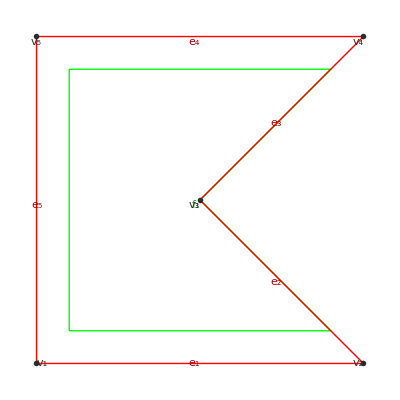

{{π/2,Null},{π/4,Null},{Null,-π/2},{Null,π/4},{π/2,Null}}

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1/2,1/2},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,1}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph;
Print[GraphGraphics[tobj]];
VertexEdgeAngles[tobj]
]
```

#### SingleVertexEdgeAngles[tobj, i0, i1] (unchecked class) TPlaneGraph

SingleVertexEdgeAngles[tobj, i0, v1] returns the sector angles around the vertex whose index is i0, list rotated so that the first sector angle in the return list lies between edge {i0, i1} and the next CCW edge around the vertex. So, if we view vertex i0 from edge {i0, i1}, the first angle in the return list is on the right side of the edge, and the last angle in the return list is on the left.

```mathematica
SingleVertexEdgeAngles::badedge="Vertex `1` is not adjacent to vertex `2`.";
```

```mathematica
SingleVertexEdgeAngles[tobj_TObj, i0_, i1_]:=Module[{verts,vva,vfi,va,vfa},
{verts,vva,vfi}=GetValues[tobj,{Vertices,VertexVertexAdjacency,VertexFaceIncidence}];
If[!MemberQ[vva⟦i0⟧,i1],Message[SingleVertexEdgeAngles::badedge,i1,i0];Abort[]];
va=AbsoluteAngle[verts⟦#⟧-verts⟦i0⟧]&/@vva⟦i0⟧;
vfa=Abs[Mod[Subtract@@#,2π,-π]]&/@Transpose[{RotateLeft[va],va}];
vfa=MapThread[If[#1==0,Null,#2]&,{vfi⟦i0⟧,vfa}];
RotateLeft[vfa,Position[vva⟦i0⟧,i1,1,1]⟦1,1⟧-1]]
```

Example. A folded vertex.

```mathematica
Module[{tobj},
tobj=SingleVertexGraph//RebuildPlaneGraph;
Print[GraphGraphics[tobj]];
SingleVertexEdgeAngles[tobj,1,2]
]//ShowExample
```

Example: 7 facets.

```mathematica
Module[{tobj},
tobj=ThreeFoldSquareGraph//RebuildPlaneGraph;
Print[GraphGraphics[tobj]];
SingleVertexEdgeAngles[tobj,10,9]
]//ShowExample
```

#### EdgeVertexAngles[tobj] (unchecked class) TPlaneGraph

EdgeVertexAngles[tobj] returns a list of the four sector angles around both vertices of all of the edges, of the form {{{α_(i,r), α_(i,l)},{α_(j,r),α_(j,l)}}, …}, where each list {{α_(i,r), α_(i,l)},{α_(j,r),α_(j,l)}} applies to edge {i,j} of tobj, and angle α_(i,r) lies to the right of vertex i, as viewed from the edge, α_(i,l) lies to its left, and similarly for the other two angles. Or, equivalently, for each edge, the first angle lies CCW of the first vertex, and then the angles circulate CCW about the edge.

```mathematica
EdgeVertexAngles[tobj_TObj]:=Module[{edges,vei,vea,ia,ib,veaa,veab},
{edges,vei}=GetValues[tobj,{Edges,VertexEdgeIncidence}];
vea=VertexEdgeAngles[tobj];
Table[
{ia,ib}=edges⟦i⟧;
veaa=RotateLeft[vea⟦ia⟧,Position[vei⟦ia⟧,i]⟦1,1⟧-1];(* edge angles around vertex ia *)
veab=RotateLeft[vea⟦ib⟧,Position[vei⟦ib⟧,i]⟦1,1⟧-1];(* edge angles around vertex ib *)
{{veaa⟦1⟧,veaa⟦-1⟧},{veab⟦1⟧,veab⟦-1⟧}}
,{i,Length[edges]}]]
```

Example

```mathematica
Module[{tobj},
tobj=SingleVertexGraph//RebuildPlaneGraph;
Print[GraphGraphics[tobj]];
Print[tobj[Edges]];
EdgeVertexAngles[tobj]
]//ShowExample
```

### TPlaneGraph slitting [TBD, this is not working yet]

#### NotchPlaneGraph[tobj, {vi1, vi2}]

NotchPlaneGraph[tobj, {vi1, vi2}] takes a TPlaneGraph and notches it by splitting an edge that terminates on the boundary into two connected edges.
	tobj is the TPlaneGraph
	{vi1, vi2} are the indices of the two vertices; v1 must be a boundary vertex, v2 must be an interior vertex connected to it.

Note: in the resulting graph. vi2 will have two adjacent vertices at the same location, which breaks the planarization algorithm in TPlaneGraph since we cannot determine the cyclic ordering of edges around that vertex purely from vertex coordinates. That means that if you call MakeTPlaneGraph on this pattern, it will fail. However, we tweak all of the TPlaneGraph contents to be properly consistent with each other.

```mathematica
NotchPlaneGraph::badvert="Vertex `1` is not a boundary vertex of `2`.";
```

```mathematica
NotchPlaneGraph::badvert1="Vertex `1` is a boundary vertex of `2`.";
```

```mathematica
NotchPlaneGraph::badedge="Edge `1` is not an edge of `2`.";
```

```mathematica
NotchPlaneGraph[tobj_TObj, {v1_,v2_}]:=Module[{verts,edges,faces,bverts,vva,vei,vfi,nvi,ei,nei,ledges,redges,lfaces,rfaces},
AssertClass[tobj,TPlaneGraph,NotchPlaneGraph];
{verts,edges,faces,bverts,vva,vei,vfi}=GetValues[tobj,{Vertices,Edges,Faces,BoundaryVertices,VertexVertexAdjacency,VertexEdgeIncidence,VertexFaceIncidence}];
If[!ContainsQ[bverts,v1],Message[NotchPlaneGraph::badvert,v1,tobj];Abort[]];
If[ContainsQ[bverts,v2],Message[NotchPlaneGraph::badvert1,v1,tobj];Abort[]];
If[!ContainsQ[edges,{v1,v2}]&&!ContainsQ[edges,{v1,v2}],Message[NotchPlaneGraph::badedge,{v1,v2},tobj];Abort[]];
AppendTo[verts,verts⟦v1⟧+{0,0}(* DEBUGGING *)];
nvi=Length[verts];(* the new vertex *)
ei=EdgeIndex[tobj,{v1,v2}];(* the old edge *)
PrintThis[ei];
AppendTo[edges,edges⟦ei⟧/.v1->nvi];(* create new edge *)
nei=Length[edges];(* index of new edge *)
(* now find all edges incident on v1 to divide them up *)
PrintThis[vei⟦v1⟧]//Hold;
PrintThis[vfi⟦v1⟧]//Hold;
With[{m=Position[vei⟦v1⟧,ei]⟦1,1⟧-1},
redges=RotateLeft[vei⟦v1⟧,m];
rfaces=RotateLeft[vfi⟦v1⟧,m]];
PrintThis[redges];
PrintThis[rfaces];
With[{m=Position[rfaces,0]⟦1,1⟧},
ledges=Take[redges,m];
redges=Drop[redges,m];
lfaces=Take[rfaces,m-1];
rfaces=Drop[rfaces,m];
];
PrintThis[ledges];
PrintThis[redges];
PrintThis[lfaces];
PrintThis[rfaces];
(* now in the right-side edges and faces, substitute the new vertex index *)
Do[edges⟦redges⟦i⟧⟧=edges⟦redges⟦i⟧⟧/.v1->nvi,{i,Length[redges]}];
Do[faces⟦rfaces⟦i⟧⟧=faces⟦rfaces⟦i⟧⟧/.v1->nvi,{i,Length[rfaces]}];
PrintThis[verts];
PrintThis[edges];
PrintThis[faces];
MakeTPlaneGraph[verts,edges,faces]
]
```

Example: a 2x2 grid, notch at bottom.

```mathematica
Module[{verts,edges,faces,tobj},
verts={{0,0},{1,0},{2,0},{0,1},{1,1},{2,1},{0,2},{1,2},{2,2}};
edges={{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{1,4},{2,5},{3,6},{4,7},{5,8},{6,9}};
faces={{1,2,5,4},{2,3,6,5},{4,5,8,7},{5,6,9,8}};
tobj=MakeTPlaneGraph[verts,edges,faces];
GraphGraphics[tobj]//Print;
tobj=NotchPlaneGraph[tobj,{2,5}];
GraphGraphics[tobj]//Print;
GetAllRules[tobj]
]//ShowExample//Hold;
```

Example: a 3x3 square grid, plus a bit.

```mathematica
Module[{n,verts,edges,tobj,tobj1},
n=3;
verts=Flatten[Table[N[{i-1,j-1}],{j,n+1},{i,n+1}],1];
edges=Join[Flatten[Table[{i+(n+1)(j-1),i+1+(n+1)(j-1)},{j,n+1},{i,n}],1],Flatten[Table[{i+(n+1)(j-1),i+(n+1)(j)},{j,n},{i,(n+1)}],1]];
edges=Join[edges,{{2,5},{2,7}}];
tobj=MakeTPlaneGraph[verts,edges];
GraphGraphics[tobj]//Print;
tobj=NotchPlaneGraph[tobj,{2,6}];
GraphGraphics[tobj]//Print;
GetAllRules[tobj]
]//ShowExample//Hold;
```

#### SlitPlaneGraph[tobj, elist] (checked class) TPlaneGraph

SlitPlaneGraph[tobj, elist] cuts a TPlaneGraph along a list of vertices.

Arguments:
	tobj — the TPlaneGraph to be slit.
	elist — a list of edge indices.

Returns a new TPlaneGraph containing the modified Vertices, Edges, and Faces. Note that any subclass information, e.g., TAssigned, is unaffected and you will have to manually add new information that corresponds to vertices and/or edges of the graph. The last Length[vlist] vertices in the returned graph are the new vertices resulting from splitting each of the vertices in vlist, in the same order. Ditto for the last Length[vlist]-1 edges.

Note that the topology of the slit edges must leave the graph connected with no holes. If this fails, then reconstructing the faces via AddTPlaneGraph will fail.

```mathematica
SlitPlaneGraph[tobj_TObj,elist_List]:=Module[{vei,vfi},
AssertClass[tobj,TPlaneGraph,SlitPlaneGraph];
{vei,vfi}=GetValues[tobj,{VertexEdgeIncidence,VertexFaceIncidence}];
PrintThis[vei];
PrintThis[vfi];

(* to come *)
]
```

Example: a 3x3 square grid.

```mathematica
Module[{n,verts,edges,tobj,tobj1},
n=3;
verts=Flatten[Table[N[{i-1,j-1}],{j,n+1},{i,n+1}],1];
edges=Join[Flatten[Table[{i+(n+1)(j-1),i+1+(n+1)(j-1)},{j,n+1},{i,n}],1],Flatten[Table[{i+(n+1)(j-1),i+(n+1)(j)},{j,n},{i,(n+1)}],1]];
tobj=MakeTPlaneGraph[verts,edges];
GraphGraphics[tobj]//Print;
SlitPlaneGraph[tobj,{4,5}];
]//ShowExample//Hold;
```

### TPlaneGraph examples

#### SquareTwist45Graph

```mathematica
Clear[SquareTwist45Graph];
AddTGraphExample[SquareTwist45Graph,Module[{verts,edges,faces},
verts={{0,0},{1,0},{2,0},{4,0},
{2,1},{4,1},
{0,2},{1,2},{3,2},{4,2},
{0,3},{2,3},
{0,4},{2,4},{3,4},{4,4}};
edges={{1,2},{2,3},{3,4},{1,7},{2,8},{3,5},{4,6},{5,6},{5,8},{5,9},{6,10},{7,8},{9,10},{7,11},{8,12},{9,12},{9,15},{10,16},{11,12},{11,13},{12,14},{13,14},{14,15},{15,16}};
MakeTGraph[verts,edges]//AddTPlaneGraph]];
```

Example

```mathematica
Module[{tobj},
tobj=SquareTwist45Graph;
GraphGraphics[tobj]
]//ShowExample
```

#### SplitSquareTwist45Graph

```mathematica
Clear[SplitSquareTwist45Graph];
AddTGraphExample[SplitSquareTwist45Graph,Module[{verts,edges,faces},
verts={{0,0},{1,0},{2,0},{4,0},
{2,1},{4,1},
{0,2},{1,2},{3,2},{4,2},
{0,3},{2,3},
{0,4},{2,4},{3,4},{4,4}};
edges={{1,2},{2,3},{3,4},{1,7},{2,8},{3,5},{4,6},{5,6},{5,8},{5,9},{6,10},{7,8},{8,9},{9,10},{7,11},{8,12},{9,12},{9,15},{10,16},{11,12},{11,13},{12,14},{13,14},{14,15},{15,16}};
MakeTGraph[verts,edges]//AddTPlaneGraph]];
```

Example

```mathematica
Module[{tobj},
tobj=SquareTwist45Graph;
GraphGraphics[tobj]
]//ShowExample
```

## Flat-folded forms

### Class TGraph2D

#### Notes

For a graph that represents a crease pattern, it is useful to represent it as a folded form using an alternate vertex embedding. We introduce the class TGraph2D with property Vertices2D to represent this alternate embedding. (This might seem ambiguous, since Vertices also represents a 2D embedding, but we will shortly introduce a 3D embedding for the folded form and call it Vertices3D; so Vertices2D and Vertices3D both represent the same thing, just different embedding dimensions for the folded form.)

#### TObj class: TGraph2D Mixin with: TGraph or subclass

TGraph2D is a mixin class that can be used to give any TGraph (or subclass of a TGraph) a second 2D embedding.

```mathematica
TGraph2D::usage="TGraph2D is a TObj class that describes a graph with a second 2D embedding.";
```

```mathematica
RegisterTClass[TGraph2D,{TGraph}];
```

#### TGraph2D properties: Vertices2D

Vertices2D is a property that gives a 2D embedding of the vertices of a TGraph.

```mathematica
Vertices2D::usage="Vertices2D is a TObj property that specifies a 2D embedding of the vertices of a graph.";
```

#### AddTGraph2DTo[tobj] AddTGraph2DTo[tobj, verts2d] MakeTGraph2D[verts, edges, faces, verts2d]

AddTGraph2DTo[tobj] takes a TGraph and sets its Vertices2D to be equal to its Vertices.

AddTGraph2DTo[tobj, verts2d] takes a TGraph and returns a TGraph2D using the specified 2D embedding verts2d.

```mathematica
AddTGraph2DTo[tobj_TObj,verts2d_List:{}]:=Module[{v2d,tobj1},
AssertClass[tobj,TGraph,AddTGraph2DTo];
v2d=If[verts2d==={},GetValue[tobj,Vertices],verts2d];
AddClassTo[tobj,TGraph2D,{Vertices2D->v2d}]]
```

Example

```mathematica
Module[{verts,edges,tobj,tobj1},
verts={{0,0},{1,0},{.5,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
tobj=AddTGraph2DTo[tobj];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

AddTGraph2D[verts2d] returns a pure function that makes adds the TGraph2D class with property value verts2d.

```mathematica
AddTGraph2D[verts2d_List:{}]:= AddTGraph2DTo[#,verts2d]&
```

Note that when chaining this constructor, you must call the function, even if you’re relying on the default empty list, i.e., do this:
	tobj // AddTGraph2D[]
not this:
	tobj // AddTGraph2D
Most of the time, though, you will have 2D vertex data and so will do this:
	tobj // AddTGraph2D[verts2d]

MakeTGraph2D[verts, edges, faces, verts2d] creates a TGraph2D from parameters.

```mathematica
MakeTGraph2D[verts_List,edges_List,faces_List:{},verts2d_List:{}]:=MakeTGraph[verts,edges,faces]//AddTGraph2D[verts2d]
```

### TGraph2D rendering

#### Graph2DGraphics[tobj, opts] (checked classes) TGraph, TGraph2D (options) Options[GenericGraphGraphics], Options[Graphics]

Graph2DGraphics[tobj, opts] takes a TGraph+TGraph2D and displays vertices, edges, and faces with labels as a Graphics object using the alternate (Vertices2D) embedding. The faces, if present, are outlined with inset polygons. We change the color from the default GraphGraphics to emphasize the difference. Options are:
	Options[GenericGraphGraphics] are passed through to GenericGraphGraphics.
	Options[Graphics] are passed through to Graphics.

```mathematica
Graph2DGraphics[tobj_TObj,opts___]:=Module[{vl,el,fl,de,fd,fc,verts2d, edges, faces,hf,gg},
AssertClass[tobj,TGraph,GraphGraphics];
AssertClass[tobj,TGraph2D,GraphGraphics];
{verts2d, edges, faces} = GetValues[tobj,{Vertices2D, Edges, Faces},AssertProperties->False];
GenericGraphGraphics[verts2d,edges,faces,EdgeColor->Darker[Magenta],opts]]
```

Example, no face data. This also shows how Graphics options are passed through to Graphics.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
tobj=MakeTGraph2D[verts,edges];
Graph2DGraphics[tobj,DirectedEdges->True,PlotLabel->"Graph2DGraphics"]
]//ShowExample
```

Example with faces, but no edge labels.

```mathematica
Module[{verts,edges,faces,tobj,fc},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
faces={{1,2,3},{3,4,1}};
fc={-1,+1};
tobj=MakeTGraph2D[verts,edges,faces];
Graph2DGraphics[tobj,FaceColoring->fc,EdgeLabels->None]
]//ShowExample
```

### TGraph2D examples

#### SingleVertexGraph2D

SingleVertexGraph2D is our SingleVertexGraph but with Vertices2D added.

```mathematica
Clear[SingleVertexGraph2D];
AddTGraphExample[SingleVertexGraph2D,Module[{tobj,verts2d},
tobj=SingleVertexGraph;
verts2d={{0,0},{1,0},{1,1},{0,1},{1,1},{1,1/√3},{-1-(3/2) (-1+1/√3),-1+(1/2) √3 (-1+1/√3)-2 (-1+(1/2) √3 (-1+1/√3))},{-1/√3,1},{1,1}}//N;
tobj//AddTGraph2D[verts2d]]];
```

Example

```mathematica
Module[{tobj},
tobj=SingleVertexGraph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

### TGraph2D interrogators

#### EdgeLengths2D[tobj] (unchecked class) TGraph2D

EdgeLengths2D[tobj] returns the lengths of the edges of tobj, but calculated from the Vertices2D embedding.

```mathematica
EdgeLengths2D[tobj_TObj]:=Module[{verts2d,edges},
{verts2d,edges}=GetValues[tobj,{Vertices2D,Edges}];
Mag[Subtract@@verts2d⟦#⟧]&/@edges]
```

```mathematica
Module[{verts,edges,eangles,tobj},
verts={{0,0},{1,0},{2,0},{3,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
tobj=MakeTGraph2D[verts,edges];
Print[GraphGraphics[tobj]];
EdgeLengths2D[tobj]
]//ShowExample
```

### TGraph2D+TPlaneGraph interrogators

#### EdgeFaceAngles2D[tobj] (unchecked class) TGraph2D, TPlaneGraph

EdgeFaceAngles2D[tobj] returns a list of the edge face angles from the 2D embedding Vertices2D, according to these rules:
	Boundary edges have an edge angle of 0 by definition.
	Edges between two faces with the same winding number have an edge angle of 0.
	Edges between two faces with opposite winding numbers have an edge angle of π.
Note that for an assigned crease pattern (see TAssigned, below) the edge angle in this case could actually be ±π. This function always returns +π. This is still sufficient to reproduce the 2D embedding using FoldGraph2D.

```mathematica
EdgeFaceAngles2D[tobj_TObj]:=Module[{verts2d,faces,efi,fwn,fpair},
{verts2d,faces,efi}=GetValues[tobj,{Vertices2D,Faces,EdgeFaceIncidence}];
fwn=WindingNumber[verts2d,#]&/@faces;(* winding number of each face *)
Table[
fpair=efi⟦i⟧;
If[MemberQ[fpair,0],
0,
If[fwn⟦fpair⟦1⟧⟧== fwn⟦fpair⟦2⟧⟧,0,π]]
,{i,Length[efi]}]]
```

Example

```mathematica
Module[{verts,verts2d,edges,tobj},
verts={{0,0},{1,0},{2,0},{3,1},{4,1},{4,0},{1,1},{0,1}};
verts2d={{0,0},{1,0},{2,0},{3,1},{3,2},{2,2},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,3},{4,7},{7,8},{8,1},{7,2}};
tobj=MakeTGraph[verts,edges]//AddTGraph2D[verts2d]//AddTPlaneGraph;
Print[GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]];
EdgeFaceAngles2D[tobj]
]//ShowExample
```

#### VertexEdgeAngles2D[tobj] (unchecked class) TGraph2D, TPlaneGraph

VertexEdgeAngles[tobj] takes a TPlaneGraph+TGraph2D and returns a list {{α_1, α_2, ...}, ...} of the sector angles around each vertex like VertexEdgeAngles, but using the Vertices2D data. As with VertexEdgeAngles, the angles for border faces are Null.

A good check on the validity of a folded form is to verify that VertexEdgeAngles and VertexEdgeAngles2D agree for all faces.

```mathematica
VertexEdgeAngles2D[tobj_TObj]:=Module[{verts,vva,vfi,va,vfa},
{verts,vva,vfi}=GetValues[tobj,{Vertices2D,VertexVertexAdjacency,VertexFaceIncidence}];
Table[
va=AbsoluteAngle[verts⟦#⟧-verts⟦i⟧]&/@vva⟦i⟧;
vfa=Abs[Mod[Subtract@@#,2π,-π]]&/@Transpose[{RotateLeft[va],va}];
MapThread[If[#1==0,Null,#2]&,{vfi⟦i⟧,vfa}]
,{i,Length[vva]}]
]
```

Example. A folded vertex.

```mathematica
Module[{tobj},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
Print[GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]];
VertexEdgeAngles2D[tobj]//N
]//ShowExample
```

Example. Compare the face angles computed from the crease pattern and folded form.

```mathematica
Module[{verts2d,tobj},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
Print[GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]];
Chop[N[VertexEdgeAngles2D[tobj]-VertexEdgeAngles[tobj]]]
]//ShowExample
```

#### SingleVertexEdgeAngles2D[tobj, i0, i1] (unchecked class) TGraph2D, TPlaneGraph

SingleVertexEdgeAngles2D[tobj, i0, v1] returns the sector angles around the vertex whose index is i0, rotated so that the first face angle returned lies between edge {i0, i1} and the next CCW edge. Same as SingleVertexEdgeAngles, but calculated from the Vertices2D data.

```mathematica
SingleVertexEdgeAngles2D::badedge="Vertex `1` is not adjacent to vertex `2`.";
```

```mathematica
SingleVertexEdgeAngles2D[tobj_TObj, i0_, i1_]:=Module[{verts,vva,vfi,va,vfa},
{verts,vva,vfi}=GetValues[tobj,{Vertices2D,VertexVertexAdjacency,VertexFaceIncidence}];
If[!MemberQ[vva⟦i0⟧,i1],Message[SingleVertexEdgeAngles2D::badedge,i1,i0];Abort[]];
va=AbsoluteAngle[verts⟦#⟧-verts⟦i0⟧]&/@vva⟦i0⟧;
vfa=Abs[Mod[Subtract@@#,2π,-π]]&/@Transpose[{RotateLeft[va],va}];
vfa=MapThread[If[#1==0,Null,#2]&,{vfi⟦i0⟧,vfa}];
RotateLeft[vfa,Position[vva⟦i0⟧,i1,1,1]⟦1,1⟧-1]]
```

Example. A folded vertex.

```mathematica
Module[{tobj},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
Print[GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]];
SingleVertexEdgeAngles2D[tobj,1,2]/°//N
]//ShowExample
```

#### EdgeVertexAngles2D[tobj] (unchecked class) TGraph2D, TPlaneGraph

EdgeVertexAngles[tobj] returns a list of the four sector angles around both vertices of all of the edges, of the form {{{α_(i,r), α_(i,l)},{α_(j,r),α_(j,l)}}, …}, where each list {{α_(i,r), α_(i,l)},{α_(j,r),α_(j,l)}} applies to edge {i,j} of tobj, and angle α_(i,r) lies to the right of vertex i, as viewed from the edge, α_(i,l) lies to its left, and similarly for the other two angles. Or, equivalently, for each edge, the first angle lies CCW of the first vertex, and then the angles circulate CCW about the edge. Same as EdgeVertexAngles, but computed from the Vertices2D data.

```mathematica
EdgeVertexAngles2D[tobj_TObj]:=Module[{edges,vei,vea,ia,ib,veaa,veab},
{edges,vei}=GetValues[tobj,{Edges,VertexEdgeIncidence}];
vea=VertexEdgeAngles2D[tobj];
Table[
{ia,ib}=edges⟦i⟧;
veaa=RotateLeft[vea⟦ia⟧,Position[vei⟦ia⟧,i]⟦1,1⟧-1];(* edge angles around vertex ia *)
veab=RotateLeft[vea⟦ib⟧,Position[vei⟦ib⟧,i]⟦1,1⟧-1];(* edge angles around vertex ib *)
{{veaa⟦1⟧,veaa⟦-1⟧},{veab⟦1⟧,veab⟦-1⟧}}
,{i,Length[edges]}]]
```

Example. A folded vertex.

```mathematica
Module[{tobj},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
Print[GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]];
Print[tobj[Edges]];
EdgeVertexAngles[tobj]
]//ShowExample
```

### Flat-folding, unfolding

#### Notes

These functions let you fold and unfold a TGraph2D that represents a crease pattern and folded form together. The first function in this section, EmbedGraph, is defined somewhat abstractly, but it allows us to use this one function to accomplish all of:
	Folding a 2D crease pattern into a 2D flat folded form
	Unfolding a 2D flat folded form into a crease pattern
	Folding a 2D crease pattern into a 3D folded form
	Unfolding a 3D folded form to its 2D crease pattern
This ability lets us visualize the folded form (either 2D or 3D) from a crease pattern and description of fold angles. It also allows us to solve inverse problems, defining a desired folded form, then unfolding them to the desired crease pattern. Of course, to go either direction, the specification of folding geometry needs to be self-consistent, satisfying developability and (for 2D forms), flat-foldability.

In Tessellatica 11.1d10, I introduced function FoldEmbedding, which is the general utility function for folding and unfolding, and is way faster than previous versions.

#### FoldEmbedding[tobj, everts, foldangles, opts] (options) StationaryFace, ShowProgress

FoldEmbedding[tobj, everts, foldangles, opts] folds a specified embedding of a TGraph.

Arguments:
	tobj — the TGraph to be folded.
	everts — the embedding vertices, could be 2D or 3D.
	foldangles — the angles on the edges.

Options:
	StationaryFace → sface, the face that remains fixed.
	ShowProgress → True | False, whether to show progress and internal structures. Useful for debugging.

Returns a new list of 3D vertices that represents the new embedding. Returned vertices are always 3D, whether or not original vertices were 2D or 3D.

Note that foldangles entries for border edges are ignored. This is made use of in FoldGraph2DAll.

```mathematica
StationaryFace::usage="StationaryFace is an option to FoldEmbedding that specifies which face remains stationary.";
```

```mathematica
ShowProgress::usage="ShowProgress is an option to FoldEmbedding (and other complex functions) that specifies to show intermediate results and internal data structures.";
```

```mathematica
Options[FoldEmbedding]={
StationaryFace->1,
ShowProgress->False
};
```

```mathematica
FoldEmbedding[tobj_TObj,everts_List,foldangles_List,opts___]:=Module[{sface,sp,dim,verts3d,tobj1,edges,faces,vei,vfi,efi,fei,ei,nf,efaces,emap,efn,dedges,vstree,bfte,kids,face,ffn,dedge,if,redge,fedge,ϕ,eface,w,q,rm,xfrm},
sface=StationaryFace/.{opts}/.Options[FoldEmbedding];
sp=ShowProgress/.{opts}/.Options[FoldEmbedding];
tobj1=If[HasClassQ[tobj,TPlaneGraph],tobj,tobj//RebuildPlaneGraph];
If[sp,Print[GraphGraphics[tobj1]]];
{edges,faces,vei,vfi,efi,fei}=GetValues[tobj1,{Edges,Faces,VertexEdgeIncidence,VertexFaceIncidence,EdgeFaceIncidence,FaceEdgeIncidence}];
(* ei[{i,j}] returns the index into edges of edge {i,j}. *)
Do[ei[edges⟦i⟧]=i;ei[Reverse[edges⟦i⟧]]=i,{i,Length[edges]}];
nf=Length[faces];
dim=Dimensions[everts]⟦2⟧;
verts3d=If[dim==3,everts,Append[#,0]&/@everts];
efaces=verts3d⟦#⟧&/@faces (* embedded faces *);
(* map pairing original edge with dual edge *)
emap=Select[Transpose[{edges,efi}],#⟦2,1⟧≠0&&#⟦2,2⟧≠0&];
If[sp,Print["emap = ",emap]];
(* efn takes a dual edge (fi,fj} and returns the corresponding original edge {i,j} *)
(efn[#⟦2⟧]=#⟦1⟧;efn[Reverse[#⟦2⟧]]=#⟦1⟧)&/@emap;
(* internal dual edges *)
dedges=Last/@emap;
If[sp,Print["internal dual edges = ",dedges]];
(* breadth-first traversal edges from the spanning tree, in reverse order *)
vstree=FindSpanningTree[{Graph[Range[nf],dedges],sface}];
bfte=Reap[BreadthFirstScan[vstree,sface,{"FrontierEdge"->Sow}]]⟦2,1⟧/.UndirectedEdge->List;
bfte=Reverse[bfte];
If[sp,Print["traversal edges = ",bfte]];
(* show the spanning tree, this time with vertices for rendering *)
If[sp,Print[Graph[vstree,VertexCoordinates->FaceCentroids[tobj1],VertexLabels->"Index",EdgeLabels->"Index",EdgeLabelStyle->Red]]];
(* children of each node of spanning tree *)
kids=Table[{i},{i,nf}];
Do[kids⟦bfte⟦i,1⟧⟧=Flatten[{kids⟦bfte⟦i,1⟧⟧,kids⟦bfte⟦i,2⟧⟧}],{i,nf-1}];
If[sp,Print["kids = ",kids]];
(* ffn[i,{j,k}] takes an undirected edge {j,k} in face i and returns the index pair into the ith face of the vertices of the corresponding directed edge. *)
Do[face=faces⟦i⟧;
With[{n=Length[face]},
Do[
ffn[i,{face⟦j⟧,face⟦Mod[j+1,n,1]⟧}]={j,Mod[j+1,n,1]};
ffn[i,{face⟦Mod[j+1,n,1]⟧,face⟦j⟧}]={j,Mod[j+1,n,1]};
,{j,Length[face]}]]
,{i,nf}];
(* for each traversal edge, apply rotation to embedded face and its children *)
Do[
dedge=bfte⟦i⟧(* directed dual edge *);
if=dedge⟦1⟧(* index of source face *);
face=faces⟦if⟧;
redge=efn[dedge](* undirected rotation edge (as pair of vertex indices) *);
fedge=ffn[if,redge](* index pair into embedded face of rotation edge *);
ϕ=foldangles⟦ei[redge]⟧;(* desired fold angle *)
eface=efaces⟦if⟧;
w=NormalizeReal[Subtract@@eface⟦fedge⟧](* rotation axis *);
q=efaces⟦if,fedge⟦1⟧⟧(* initial point of rotation axis *);
rm=RotationMatrix3Du[ϕ,w](* fully evaluate rotation matrix *);
xfrm=q+rm.(#-q)&;
If[sp,Print[{"dedge"->dedge,"if"->if,"face"->face,"redge"->redge,"fedge"->fedge,"eface"->eface,"ϕ"->ϕ,"w"->w,"q"->q}]];
Do[efaces⟦kids⟦dedge⟦2⟧,j⟧⟧=xfrm/@efaces⟦kids⟦dedge⟦2⟧,j⟧⟧,{j,Length[kids⟦dedge⟦2⟧⟧]}];
,{i,nf-1}];
If[sp,Print[Graphics3D[Line[AppendFirst[#]]&/@efaces]]];
(* rebuild verts3d from embedded faces *)
Do[Do[verts3d⟦faces⟦i,j⟧⟧=efaces⟦i,j⟧,{j,Length[faces⟦i⟧]}],{i,nf}];
verts3d]
```

Example. A 2D shape.

```mathematica
Module[{tobj,foldangles,newverts},
tobj=SimpleSquareTwistGraph//RebuildPlaneGraph;
foldangles={π,π,π,π,π,-π,π,-π,π,-π,π,-π,0,0,0,0,0,0,0,0,0,0,0,0};
newverts=FoldEmbedding[tobj,tobj[Vertices],foldangles];
tobj=tobj//AddTGraph2D[Drop[#,-1]&/@newverts];
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

#### FoldGraph2D[tobj, foldangles, opts] (checked class) TGraph (options) StationaryFace, ShowProgress

FoldGraph2D[tobj, foldangles, opts] folds a TGraph according to a set of fold angles.

Arguments:
	tobj — the TGraph being folded.
	foldangles — an array of fold angles for each edge. Should be 0 for unfolded and border, ±π for folded edges.

Options:
	StationaryFace → sface, the index of the face whose position remains unchanged.
	ShowProgress → True | False, whether to show progress and internal structures. Useful for debugging.

Returns a TGraph2D with the new embedding in property Vertices2D. Any existing Vertices2D data is replaced.

The original embedding should obey the Kawasaki-Justin Condition for all folded creases. If it doesn’t, no error will be generated but the results may be unreliable/unpredictable.

Note that although we only need a TGraph, not necessarily a full TPlaneGraph, if it isn’t a TPlaneGraph, index StationaryFace will apply to the default face list computed by TPlaneGraph, which might not be the same as the current Faces property.

```mathematica
Options[FoldGraph2D]={
StationaryFace->1
};
```

```mathematica
FoldGraph2D[tobj_TObj,foldangles_List,opts___]:=Module[{tobj1,verts,edges,faces,sface,v,e,f,m,p,el,ea,vfa,verts2d},
AssertClass[tobj,TGraph,FoldGraph2D];
verts2d=Drop[#,-1]&/@FoldEmbedding[tobj,tobj[Vertices],foldangles,opts];
If[HasClassQ[tobj,TGraph2D],tobj//ReplaceProperty[Vertices2D->verts2d],tobj//AddTGraph2D[verts2d]]]
```

Example. A folded vertex; show details.

```mathematica
Module[{tobj,foldangles},
tobj=SingleVertexGraph;
foldangles={π,π,-π,π,0,0,0,0,0,0,0,0};
tobj=FoldGraph2D[tobj,foldangles,ShowProgress->True];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj]
}]]//ShowExample
```

Example. Cross-pleated square.

```mathematica
Module[{tobj,foldangles},
tobj=CrossPleatedSquareGraph;
foldangles={0,0,0,π,π,π,-π,-π,-π,0,0,0,0,π,-π,0,0,-π,π,0,0,π,-π,0};
tobj=FoldGraph2D[tobj,foldangles];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj]
}]]//ShowExample
```

Example. A square twist.

```mathematica
Module[{tobj,foldangles},
tobj=SimpleSquareTwistGraph;
foldangles={π,π,π,π,π,-π,π,-π,π,-π,π,-π,0,0,0,0,0,0,0,0,0,0,0,0};
tobj=FoldGraph2D[tobj,foldangles];
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

Two side-by-side twists.

```mathematica
Module[{angles,tobj},
angles={-π,-π,-π,-π,-π,-π,-π,-π,-π,-π,-π,π,π,π,π,π,π,π,π,π,π,π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
tobj=TObj[{TClasses -> {TGraph, TPlaneGraph}, Vertices -> {{0.6, 0.}, {0.7665750576834912, 0.48086077196920557}, {0.5191392280307945, 0.7665750576834912}, {0.6, 1.}, {0.23342494231650882, 0.5191392280307945}, {0., 0.6}, {0.48086077196920557, 0.23342494231650882}, {1.6, 0.}, {1.7665750576834913, 0.48086077196920557}, {2., 0.6}, {1.5191392280307945, 0.7665750576834912}, {1.6, 1.}, {1.233424942316509, 0.5191392280307945}, {1.4808607719692055, 0.23342494231650882}, {0.4, 0.}, {0.4, 1.}, {0., 0.4}, {1.4, 0.}, {2., 0.4}, {1.4, 1.}, {0., 0.}, {1., 0.}, {1., 1.}, {0., 1.}, {2., 0.}, {2., 1.}}, Edges -> {{1, 2}, {4, 3}, {3, 5}, {6, 5}, {5, 7}, {8, 9}, {10, 11}, {12, 11}, {11, 13}, {13, 14}, {3, 13}, {15, 7}, {7, 2}, {2, 3}, {16, 5}, {17, 7}, {18, 14}, {14, 9}, {19, 9}, {9, 11}, {20, 13}, {2, 14}, {15, 1}, {4, 16}, {6, 17}, {21, 15}, {17, 21}, {1, 22}, {23, 4}, {24, 6}, {16, 24}, {18, 8}, {19, 10}, {12, 20}, {22, 18}, {25, 19}, {8, 25}, {26, 12}, {10, 26}, {20, 23}}, Faces -> {{1, 2, 7, 15}, {4, 3, 13, 20, 23}, {3, 5, 7, 2}, {6, 5, 16, 24}, {8, 9, 14, 18}, {10, 11, 9, 19}, {12, 11, 10, 26}, {11, 13, 14, 9}, {15, 7, 17, 21}, {16, 5, 3, 4}, {17, 7, 5, 6}, {18, 14, 2, 1, 22}, {19, 9, 8, 25}, {20, 13, 11, 12}, {2, 14, 13, 3}}, InteriorVertices -> {2, 3, 5, 7, 9, 11, 13, 14}, BoundaryVertices -> {22, 18, 8, 25, 19, 10, 26, 12, 20, 23, 4, 16, 24, 6, 17, 21, 15, 1}, BoundaryEdges -> {35, 32, 37, 36, 33, 39, 38, 34, 40, 29, 24, 31, 30, 25, 27, 26, 23, 28}, BoundaryFaces -> {12, 5, 13, 13, 6, 7, 7, 14, 2, 2, 10, 4, 4, 11, 9, 9, 1, 12}, VertexVertexAdjacency -> {{22, 2, 15}, {7, 1, 14, 3}, {5, 2, 13, 4}, {3, 23, 16}, {7, 3, 16, 6}, {17, 5, 24}, {15, 2, 5, 17}, {25, 9, 18}, {14, 8, 19, 11}, {19, 26, 11}, {13, 9, 10, 12}, {11, 26, 20}, {14, 11, 20, 3}, {18, 9, 13, 2}, {1, 7, 21}, {5, 4, 24}, {21, 7, 6}, {8, 14, 22}, {25, 10, 9}, {13, 12, 23}, {15, 17}, {18, 1}, {20, 4}, {6, 16}, {19, 8}, {10, 12}}, VertexEdgeIncidence -> {{28, 1, 23}, {13, 1, 22, 14}, {3, 14, 11, 2}, {2, 29, 24}, {5, 3, 15, 4}, {25, 4, 30}, {12, 13, 5, 16}, {37, 6, 32}, {18, 6, 19, 20}, {33, 39, 7}, {9, 20, 7, 8}, {8, 38, 34}, {10, 9, 21, 11}, {17, 18, 10, 22}, {23, 12, 26}, {15, 24, 31}, {27, 16, 25}, {32, 17, 35}, {36, 33, 19}, {21, 34, 40}, {26, 27}, {35, 28}, {40, 29}, {30, 31}, {36, 37}, {39, 38}}, VertexFaceIncidence -> {{12, 1, 0}, {1, 12, 15, 3}, {3, 15, 2, 10}, {2, 0, 10}, {3, 10, 4, 11}, {11, 4, 0}, {1, 3, 11, 9}, {13, 5, 0}, {5, 13, 6, 8}, {0, 7, 6}, {8, 6, 7, 14}, {7, 0, 14}, {8, 14, 2, 15}, {5, 8, 15, 12}, {1, 9, 0}, {10, 0, 4}, {9, 11, 0}, {5, 12, 0}, {0, 6, 13}, {14, 0, 2}, {9, 0}, {12, 0}, {0, 2}, {4, 0}, {13, 0}, {0, 7}}, EdgeEdgeAdjacency -> {{{23, 28}, {22, 14, 13}}, {{29, 24}, {3, 14, 11}}, {{14, 11, 2}, {15, 4, 5}}, {{30, 25}, {5, 3, 15}}, {{3, 15, 4}, {16, 12, 13}}, {{32, 37}, {19, 20, 18}}, {{33, 39}, {8, 9, 20}}, {{38, 34}, {9, 20, 7}}, {{20, 7, 8}, {21, 11, 10}}, {{9, 21, 11}, {22, 17, 18}}, {{2, 3, 14}, {10, 9, 21}}, {{26, 23}, {13, 5, 16}}, {{5, 16, 12}, {1, 22, 14}}, {{13, 1, 22}, {11, 2, 3}}, {{24, 31}, {4, 5, 3}}, {{25, 27}, {12, 13, 5}}, {{35, 32}, {18, 10, 22}}, {{10, 22, 17}, {6, 19, 20}}, {{36, 33}, {20, 18, 6}}, {{18, 6, 19}, {7, 8, 9}}, {{34, 40}, {11, 10, 9}}, {{14, 13, 1}, {17, 18, 10}}, {{12, 26}, {28, 1}}, {{2, 29}, {31, 15}}, {{4, 30}, {27, 16}}, {{27}, {23, 12}}, {{16, 25}, {26}}, {{1, 23}, {35}}, {{40}, {24, 2}}, {{31}, {25, 4}}, {{15, 24}, {30}}, {{17, 35}, {37, 6}}, {{19, 36}, {39, 7}}, {{8, 38}, {40, 21}}, {{28}, {32, 17}}, {{37}, {33, 19}}, {{6, 32}, {36}}, {{39}, {34, 8}}, {{7, 33}, {38}}, {{21, 34}, {29}}}, EdgeFaceIncidence -> {{1, 12}, {2, 10}, {3, 10}, {4, 11}, {3, 11}, {5, 13}, {6, 7}, {7, 14}, {8, 14}, {8, 15}, {2, 15}, {1, 9}, {1, 3}, {3, 15}, {4, 10}, {9, 11}, {5, 12}, {5, 8}, {6, 13}, {6, 8}, {2, 14}, {12, 15}, {1, 0}, {10, 0}, {11, 0}, {9, 0}, {9, 0}, {12, 0}, {2, 0}, {4, 0}, {4, 0}, {5, 0}, {6, 0}, {14, 0}, {12, 0}, {13, 0}, {13, 0}, {7, 0}, {7, 0}, {2, 0}}, FaceEdgeIncidence -> {{1, 13, 12, 23}, {2, 11, 21, 40, 29}, {3, 5, 13, 14}, {4, 15, 31, 30}, {6, 18, 17, 32}, {7, 20, 19, 33}, {8, 7, 39, 38}, {9, 10, 18, 20}, {12, 16, 27, 26}, {15, 3, 2, 24}, {16, 5, 4, 25}, {17, 22, 1, 28, 35}, {19, 6, 37, 36}, {21, 9, 8, 34}, {22, 10, 11, 14}}}];
tobj=FoldGraph2D[tobj,angles];
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

#### UnfoldGraph2D[tobj, opts] (checked class) TGraph2D (options) StationaryFace, ShowProgress

UnfoldGraph2D[tobj, opts] unfolds a TGraph2D from the Vertices2D embedding in the same way that FoldGraph2D folded it from the Vertices embedding. The stationary face position and orientation is taken from the 2D embedding.

Arguments:
	tobj — the TGraph2D to be unfolded.

Options:
	StationaryFace → sface, the index of the face whose position remains unchanged.
	ShowProgress → True | False, whether to show progress and internal structures. Useful for debugging.

Returns a TGraph2D with the new embedding in property Vertices. Any existing Vertices data is replaced.

```mathematica
Options[UnfoldGraph2D]={
StationaryFace->1
};
```

```mathematica
UnfoldGraph2D[tobj_TObj,opts___]:=Module[{foldangles,verts},
AssertClass[tobj,TGraph2D,UnfoldGraph2D];
foldangles=EdgeFaceAngles2D[If[HasClassQ[tobj,TPlaneGraph],tobj,tobj//RebuildPlaneGraph]];
verts=Drop[#,-1]&/@FoldEmbedding[tobj,tobj[Vertices2D],foldangles,opts];
tobj//ReplaceProperty[Vertices->verts]]
```

Example. A folded vertex. Fold it up, then unfold it again.

```mathematica
Module[{foldangles,tobj,tobj1},
foldangles={π,π,-π,π,0,0,0,0,0,0,0,0};
tobj=SingleVertexGraph;
tobj=FoldGraph2D[tobj,foldangles];
tobj1=UnfoldGraph2D[tobj,ShowProgress->False];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj],
GraphGraphics[tobj1]
}]]//ShowExample
```

Example. Cross-pleated square.

```mathematica
Module[{foldangles,tobj,tobj1},
tobj=CrossPleatedSquareGraph;
foldangles={0,0,0,π,π,π,-π,-π,-π,0,0,0,0,π,-π,0,0,-π,π,0,0,π,-π,0};
tobj=FoldGraph2D[tobj,foldangles];
tobj1=UnfoldGraph2D[tobj];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj],
GraphGraphics[tobj1]
}]]//ShowExample
```

Example. A square twist.

```mathematica
Module[{foldangles,tobj,tobj1},
tobj=SimpleSquareTwistGraph;
foldangles={π,π,π,π,
π,-π,π,-π,π,-π,π,-π,
0,0,0,0,0,0,0,0,0,0,0,0};
tobj=FoldGraph2D[tobj,foldangles];
tobj1=UnfoldGraph2D[tobj];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj],
GraphGraphics[tobj1]
}]]//ShowExample
```

#### FoldGraph2DAll[tobj, opts] (checked class) TGraph (options) StationaryFace, ShowProgress

FoldGraph2DAll[tobj, opts] folds a TGraph on all internal edges.

Arguments:
	tobj — the TGraph2D to be unfolded.

Options:
	StationaryFace → sface, the index of the face whose position remains unchanged.
	ShowProgress → True | False, whether to show progress and internal structures. Useful for debugging.

Returns: the new TGraph2D with folded form as property Vertices2D.

FoldGraph2DAll was the original flat-folding routine; it folds on every interior crease. The new and improved version FoldGraph2D requires explicit fold angles, but that means you can included unfolded creases in the crease pattern and they will be handled properly.

The original embedding should obey the Kawasaki-Justin Condition; if it doesn’t, no error will be generated but the resulting embedding will be incorrect.

```mathematica
FoldGraph2DAll[tobj_TObj,opts___]:=FoldGraph2D[tobj,Table[π,{Length[tobj[Edges]]}],opts]
```

Example

```mathematica
Module[{tobj,foldangles},
tobj=SingleVertexGraph;
foldangles={π,π,-π,π,0,0,0,0,0,0,0,0};
tobj=FoldGraph2DAll[tobj];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj]
}]]//ShowExample
```

### Flopping, rotation

#### FlopGraph2D[tobj, opts] (checked class) TGraph2D (options) FlopDirection

FlopGraph2D[tobj, opts] flops the Vertices2D of the given TGraph2D, as if you had turned over the folded form.

Options:
	FlopDirection → Horizontal | Vertical, specifies the direction (not axis) of flopping.

Note that this ONLY applies to the folded form; if you want to turn over the CP, use FlopGraph.

```mathematica
Options[FlopGraph2D]={
FlopDirection->Horizontal
};
```

```mathematica
FlopGraph2D[tobj_, opts___]:=Module[{fd,verts2d,ctr},
AssertClass[tobj,TGraph2D,FlopGraph2D];
fd=FlopDirection/.{opts}/.Options[FlopGraph2D];
hori=(fd===Horizontal);
verts2d=GetValue[tobj,Vertices2D];
ctr={(Max[#1]+Min[#1])/2,(Max[#2]+Min[#2])/2}&@@Transpose[verts2d];
If[fd===Horizontal,
verts2d=ctr+ReflectionYMatrix2D.(#-ctr)&/@verts2d,
verts2d=ctr+ReflectionXMatrix2D.(#-ctr)&/@verts2d];
tobj//ReplaceProperty[Vertices2D->verts2d]]
```

Example. A folded vertex. Fold it up, then flop vertically and horizontally and show all results.

```mathematica
Module[{tobj,tobjh,tobjv},
tobj=SingleVertexGraph2D;
tobjh=FlopGraph2D[tobj];
tobjv=FlopGraph2D[tobj,FlopDirection->Vertical];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj],
Graph2DGraphics[tobjh],
Graph2DGraphics[tobjv]
}]]//ShowExample
```

#### RotateGraph2D[tobj, ϕ] (checked class) TGraph2D

RotateGraph2D[tobj, ϕ] rotates the folded form of a graph through angle ϕ about its centroid.

```mathematica
RotateGraph2D[tobj_,ϕ_]:=Module[{verts2d,ctr,rr},
AssertClass[tobj,TGraph2D,RotateGraph2D];
verts2d=GetValue[tobj,Vertices2D];
ctr={(Max[#1]+Min[#1])/2,(Max[#2]+Min[#2])/2}&@@Transpose[verts2d];
rr=RotationMatrix2D[ϕ];
verts2d=ctr+rr.(#-ctr)&/@verts2d;
tobj//ReplaceProperty[Vertices2D->verts2d]]
```

Example. A folded vertex. Fold it up, then flop vertically and horizontally and show all results.

```mathematica
Module[{tobj,tobjr},
tobj=SingleVertexGraph2D;
tobjr=RotateGraph2D[tobj,15°];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj],
Graph2DGraphics[tobjr]
}]]//ShowExample
```

### More TGraph2D examples

#### CrossPleatedSquareGraph2D

CrossPleatedSquareGraph2D is a TGraph2D that is a cross-pleated square.

```mathematica
Clear[CrossPleatedSquareGraph2D];
AddTGraphExample[CrossPleatedSquareGraph2D,Module[{tobj},
tobj=CrossPleatedSquareGraph;
FoldGraph2DAll[tobj]]];
```

Example

```mathematica
Module[{tobj},
tobj=CrossPleatedSquareGraph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

#### SimpleSquareTwistGraph2D

SimpleSquareTwistGraph2D is a TGraph2D that is a square twist.

```mathematica
Clear[SimpleSquareTwistGraph2D];
AddTGraphExample[SimpleSquareTwistGraph2D,Module[{tobj},
tobj=SimpleSquareTwistGraph;
FoldGraph2DAll[tobj]]];
```

Example

```mathematica
Module[{tobj},
tobj=SimpleSquareTwistGraph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

#### SquareTwist45Graph2D

```mathematica
Clear[SquareTwist45Graph2D];
AddTGraphExample[SquareTwist45Graph2D,Module[{tobj},
tobj=SquareTwist45Graph;
FoldGraph2DAll[tobj]]];
```

Example

```mathematica
Module[{tobj},
tobj=SquareTwist45Graph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

#### SplitSquareTwist45Graph2D

We can’t use FoldGraph2DAll on SplitSquareTwist45Graph because one of the folds remains unfolded, but we can build this by modifying SquareTwist45Graph2D.

```mathematica
Clear[SplitSquareTwist45Graph2D];
AddTGraphExample[SplitSquareTwist45Graph2D,Module[{tobj,edges},
tobj=SplitSquareTwist45Graph;
tobj=SquareTwist45Graph2D;
edges=Append[GetValue[tobj,Edges],{8,9}];
tobj//ReplaceProperty[Edges->edges]//RebuildPlaneGraph]];
```

Example

```mathematica
Module[{tobj},
tobj=SplitSquareTwist45Graph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

#### BirdBaseGraph2D

BirdBaseGraph2D gives the folded form of an origami Bird Base. Because folding it involves petal folds, we have to construct it in the already-folded state. (OK, yes, it’s technically possible to create a Bird Base using just mountains, valleys, and reverse folds, but this is still probably easier.)

```mathematica
Clear[BirdBaseGraph2D];
AddTGraphExample[BirdBaseGraph2D,Module[{h,verts,edges,a,b,c,d,e,f,verts2d},
h=.5(√2-1);
verts={{0,0},{.5,0},{1,0},
{.5,h},
{0,.5},{h,.5},{.5,.5},{1-h,.5},{1,.5},
{.5,1-h},
{0,1},{.5,1},{1,1},
{.5-h/√2,.5-h/√2},{.5+h/√2,.5+h/√2}};
edges={{1,2},{2,3},{1,5},{1,6},{1,4},{2,4},{3,4},{3,8},{3,9},
{4,14},{14,6},{4,7},{4,8},
{5,6},{6,7},{7,8},{8,9},
{5,11},{6,11},{6,10},{7,10},{8,15},{15,10},{8,13},{9,13},
{10,11},{10,12},{10,13},
{11,12},{12,13},
{1,14},{14,7},{7,15},{15,13}};
(* folded form vertices *)
a={0,0};b={-h,.5};c={0,.5};d={h,.5};e={0,.5+h};f={0,1};
verts2d={a,c,f,b,c,
b,e,d,c,d,
f,c,a,c,c};
MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph2D[verts2d]]];
```

Example

```mathematica
Module[{tobj},
tobj=BirdBaseGraph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

## Sequential flat-folding

### Class TSplitGraph2D

#### Notes

One of the ways of generating a complex TGraph2D (a description of a flat-folded shape) is to start with a simpler version and then sequentially add folds to it. Class TSplitTGraph2D is a class that represents an intermediate stage of this flat-folding process: it describes an interaction between a TGraph2D and a superimposed fold line that will split some faces and edges. TSplitGraph2D describes the state with splitting information included but not actually applied yet. This gives us the opportunity to adjust the splitting information so as to only fold certain parts of the model. The fold line and splitting information is encapsulated in this class.

#### TObj class: TSplitGraph2D Inherits from: TGraph2D

TSplitGraph2D is a subclass that can be used to give any TGraph2D a fold line and splitting information.

```mathematica
TSplitGraph2D::usage="TSplitGraph2D is a TObj class that describes a flat folded form with an interacting fold line and splitting information.";
```

```mathematica
RegisterTClass[TSplitGraph2D,{TGraph2D}];
```

#### TSplitGraph2D properties: SplitFoldLine SplitInfo

SplitFoldLine is a property that describes the position and direction of a fold line superimposed on the folded form. It consists of a list {p, r} where p is a point on the line and r is a direction vector for the line.

```mathematica
SplitFoldLine::usage="SplitFoldLine is a TObj property that specifies a fold line on a TGraph2D";
```

SplitInfo is a collection of data that describes splitting that could happen to a TGraph2D.

```mathematica
SplitInfo::usage="SplitInfo is a TObj property that specifies splitting activity on a TGraph2D";
```

SplitInfo is a structured list of the form {vfinfo, efinfo, esinfo, fsinfo} where
	vfinfo is a list of indices of vertices hit by the fold line.
	efinfo is a list of indices of edges that are collinear with the fold line.
	esinfo is a list of pairs {i, t} of edges that are split by the fold line in their interior. i is the edge index, t is the relative distance along the edge where the split occurs.
	fsinfo is a list of data {i, {fj, j}, {fk, k}} of faces that are split by a fold line, where
		i is the index of a face to be split,
		{fj, j} specifies one endpoint of the new face-splitting edge. If fj==0, it’s a vertex and j is the vertex index. If fj==1, it’s a split edge and j is the edge index.
		{fk, k} specifies the other endpoint of the new face-splitting edge in the same way.

#### MakeSplitGraph2D[tobj, {p, r}, opts] (checked classes) TGraph2D, TPlaneGraph (options) PtOnLineTolerance

MakeSplitGraph2D[tobj, {p,r}, opts] takes a TGraph2D+TPlaneGraph and adds information about a fold line, which vertices and edges are hit by the fold line, and which edges and faces would be split.

Arguments:
	tobj — the TGraph2D+TPlaneGraph that represents the initial folded state.
	p — a point on the desired fold line.
	r — a vector along the desired fold line.

Options:
	PtOnLineTolerance → tol, the tolerance on whether a vertex is hit by the fold line; passed through to PtOnLineQ.

Returns a TSplitGraph2D, with the new properties SplitFoldLine and SplitInfo.

The SplitInfo property gives us a description of what would happen if we folded the entire model everywhere that it intersected the fold line. Often, though, we will only want to fold a subset of the model. MakeSplitGraph2D puts the splitting information in a form that will be relatively easy to visualize and construct a subset that describes just the part of the model that we want to fold.

See above for the structure of the SplitInfo property. Note that if an edge is represented in esinfo, that is a guarantee that its endpoints are not in vfinfo, and vice-versa. Similarly, if an edge is represented in efinfo, that is a guarantee that any face incident to that edge is not in fsinfo and vice-versa.

We also rely on the behavior that faces are non-concave, so that a face contains exactly 0 or 2 split elements (vertices or edges). If, for some reason this condition isn’t satisfied, we detect it and bail, rather than trying to forge onward and make things worse.

```mathematica
MakeSplitGraph2D::badsplit="MakeSplitGraph2D failed to split face `1` based on vfinfo=`2`, esinfo=`3`. Intersection list is flist=`4`";
```

```mathematica
Options[MakeSplitGraph2D]={
PtOnLineTolerance->(PtOnLineTolerance/.Options[PtOnLineQ])
};
```

```mathematica
MakeSplitGraph2D[tobj_TObj,{p_List,r_List},opts___]:=Module[{tol,vfinfo,efinfo,esinfo,fsinfo,flist,verts2d,edges,faces,fei,r0,d0,tpair},
tol=PtOnLineTolerance/.{opts}/.Options[MakeSplitGraph2D];
AssertClasses[tobj,{TGraph2D,TPlaneGraph},MakeSplitGraph2D];
{verts2d,edges,faces,fei}=GetValues[tobj,{Vertices2D,Edges,Faces,FaceEdgeIncidence}];
(* vertices on fold line *)
vfinfo={};
Do[
If[PtOnLineQ[verts2d⟦i⟧,{p,r},opts],AppendTo[vfinfo,i]],{i,Length[verts2d]}];
(* edges on fold line (has both vertices on fold line) *)
efinfo={};
Do[If[ContainsAll[vfinfo,edges⟦i⟧],AppendTo[efinfo,i]],{i,Length[edges]}];
(* edges split by fold line *)
esinfo={};
Do[If[DisjointQ[vfinfo,edges⟦i⟧],
{r0,d0,tpair}=LineSegmentMedialInfo[{p,p+r},verts2d⟦edges⟦i⟧⟧];
If[2d0≤tol,AppendTo[esinfo,{i,tpair⟦2⟧}]]],{i,Length[edges]}];
(* faces split by fold line *)
fsinfo={};
Do[
(* If any face edge is on the fold line, no need to consider further *)
If[IntersectingQ[fei⟦i⟧,efinfo],Continue[]];
flist={};
Do[If[MemberQ[vfinfo,faces⟦i,j⟧],AppendTo[flist,{0,faces⟦i,j⟧}]],{j,Length[faces⟦i⟧]}];
Do[If[MemberQ[First/@esinfo,fei⟦i,j⟧],AppendTo[flist,{1,fei⟦i,j⟧}]],{j,Length[fei⟦i⟧]}];
(* ignore faces that don't hit the fold line anywhere *)
If[Length[flist]==0,Continue[]];
(* ignore faces that hit the fold line at only one vertex *)
If[Length[flist]==1&&flist⟦1,1⟧==0,Continue[]];
(* faces that hit the fold line at two places should be split *)
If[Length[flist]==2,
AppendTo[fsinfo,Join[{i},flist]],
(* otherwise, bad number of intersections with face *)
Message[MakeSplitGraph2D::badsplit,i,vfinfo,esinfo,flist];Abort[]]
,{i,Length[faces]}];AddClassTo[tobj,TSplitGraph2D,{SplitFoldLine->{p,r},SplitInfo->{vfinfo,efinfo,esinfo,fsinfo}}]]
```

Example. A single vertex that has all types of SplitInfo data.

```mathematica
Module[{tobj,f1,f2,sinfo},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.1};
f2={0,1.5};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
GraphicsRow[{
GraphGraphics[tobj],
Show[Graph2DGraphics[tobj],Graphics[{Style[Line[{f1,f2}],Lighter[Blue]],Style[Point/@{f1,f2},Blue,PointSize[.015]]}]]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm
]//ShowExample
```

### TSplitGraph2D rendering

#### SplitGraphGraphics[tobj, opts] (checked class) TSplitGraph2D (options) Options[GraphGraphics]

SplitGraphGraphics[tobj, pfinfo, opts] produces a Graphics object that gives a visualization of the splitting-by-fold in the crease pattern by drawing all of the folded edges and face splitting lines on top of the GraphGraphics representation, that latter with their corresponding indices.

Arguments:
	tobj — the TSplitGraph2D

Options:
	Options[GraphGraphics] are passed through.

Returns a Graphics object that displays the crease pattern graph, all folded edges, and all face-splitting lines.

Note that while the splitting folds (of course) overlap in the folded form, they will be distinct in the crease pattern, allowing us to visually identify the subset that we would like to actually fold on.

```mathematica
SplitGraphGraphics[tobj_TObj,opts___]:=Module[{verts,edges,sinfo,vfinfo,efinfo,esinfo,fsinfo,et,elems,fj,j,p1,p2,q1,q2},
AssertClass[tobj,TSplitGraph2D,SplitGraphGraphics];
{verts,edges,sinfo}=GetValues[tobj,{Vertices,Edges,SplitInfo}];
{vfinfo,efinfo,esinfo,fsinfo}=sinfo;
(* make a lookup table from split edge index to its split parameter *)
(et[#⟦1⟧]=#⟦2⟧)&/@esinfo;
elems=Join[
(* folded edges, no labels needed *)
Table[
{p1,p2}=verts⟦edges⟦efinfo⟦i⟧⟧⟧;
Style[Line[{p1,p2}],Blue]
,{i,Length[efinfo]}],
(* face-splitting edges, label with face index *)
Table[
{fj,j}=fsinfo⟦i,2⟧;
p1=If[fj==0,verts⟦j⟧,
{q1,q2}=verts⟦edges⟦j⟧⟧;
q1+et[j](q2-q1)];
{fj,j}=fsinfo⟦i,3⟧;
p2=If[fj==0,verts⟦j⟧,
{q1,q2}=verts⟦edges⟦j⟧⟧;
q1+et[j](q2-q1)];
{Style[Line[{p1,p2}],Blue],
Style[LabelPt[Subscript["f", fsinfo⟦i,1⟧],.5p1+.5p2],Darker[Blue]]}
,{i,Length[fsinfo]}]];
Show[GraphGraphics[tobj,opts],Graphics[elems]]]
```

Example. This will now show the fold lines on the crease pattern, with indices for face-splitting edges.

```mathematica
Module[{tobj,f1,f2,sinfo},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.1};
f2={0,1.5};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
GraphicsRow[{
SplitGraphGraphics[tobj],
Show[Graph2DGraphics[tobj],Graphics[{Style[Line[{f1,f2}],Lighter[Blue]],Style[Point/@{f1,f2},Blue,PointSize[.015]]}]]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm
]//ShowExample
```

#### SplitGraph2DGraphics[tobj, opts] (checked class) TSplitGraph2D (options) Options[Graph2DGraphics]

SplitGraph2DGraphics[tobj, pfinfo, opts] produces a Graphics object that gives a visualization of the splitting-by-fold in the folded form by drawing all of the folded edges and face splitting lines on top of the Graph2DGraphics representation and overlaying that on the fold line.

Unlike in SplitGraphGraphics, no labels are added for new edges, since they’d all overlap one another.

Arguments:
	tobj — the TSplitGraph2D

Options:
	Options[Graph2DGraphics] are passed through.

Returns a Graphics object that displays the folded form graph, all folded edges, and all face-splitting lines.

```mathematica
SplitGraph2DGraphics[tobj_TObj,opts___]:=Module[{verts2d,edges,sfl,sinfo,p,r,vfinfo,efinfo,esinfo,fsinfo,et,elems,fj,j,p1,p2,q1,q2},
AssertClass[tobj,TSplitGraph2D,SplitGraph2DGraphics];
{verts2d,edges,sfl,sinfo}=GetValues[tobj,{Vertices2D,Edges,SplitFoldLine,SplitInfo}];
{p,r}=sfl;
{vfinfo,efinfo,esinfo,fsinfo}=sinfo;
(* make a lookup table from split edge index to its split parameter *)
(et[#⟦1⟧]=#⟦2⟧)&/@esinfo;
elems=Join[
(* folded edges, no labels needed *)
Table[
{p1,p2}=verts2d⟦edges⟦efinfo⟦i⟧⟧⟧;
Style[Line[{p1,p2}],Blue]
,{i,Length[efinfo]}],
(* face-splitting edges, label with face index *)
Table[
{fj,j}=fsinfo⟦i,2⟧;
p1=If[fj==0,verts2d⟦j⟧,
{q1,q2}=verts2d⟦edges⟦j⟧⟧;
q1+et[j](q2-q1)];
{fj,j}=fsinfo⟦i,3⟧;
p2=If[fj==0,verts2d⟦j⟧,
{q1,q2}=verts2d⟦edges⟦j⟧⟧;
q1+et[j](q2-q1)];
Style[Line[{p1,p2}],Blue]
,{i,Length[fsinfo]}]];
Show[Graphics[Style[Line[{p,p+r}],LightGray]],Graph2DGraphics[tobj,opts],Graphics[elems]]]
```

Example. This will now show the fold lines on the crease pattern, with indices for face-splitting edges, and the actual fold lines on the folded form.

```mathematica
Module[{tobj,f1,f2,sinfo},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.2};
f2={0,1.4};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm
]//ShowExample
```

### Sequential flat-folding

#### FilterSplitGraph2D[tobj, eflist, fslist] (checked class) TSplitGraph2D

FilterSplitGraph2D[tobj, eflist, fslist] takes a TSplitGraph2D and returns a new version that contains a subset of the splitting information specified by the desired folded edges and split faces.

Arguments:
	tobj — the TSplitGraph2D to be modified.
	eflist — a list of the desired folded edges, given as indices
	fslist — a list of the desired split faces, given as indices

Returns a new TSplitGraph2D with modified SplitInfo property.

```mathematica
FilterSplitGraph2D[tobj_TObj,eflist_List,fslist_List]:=Module[{edges,sinfo,vfinfo,efinfo,esinfo,fsinfo,vfinfo1,efinfo1,esinfo1,fsinfo1,vfe,vsf,esf},
AssertClasses[tobj,{TGraph2D,TPlaneGraph},FilterSplitGraph2D];
{edges,sinfo}=GetValues[tobj,{Edges,SplitInfo}];
{vfinfo,efinfo,esinfo,fsinfo}=sinfo;
efinfo1=eflist;
fsinfo1=Select[fsinfo,MemberQ[fslist,#⟦1⟧]&];
(* vertices that are part of folded edges *)
vfe=Union[Flatten[edges⟦efinfo1⟧]];
(* vertices that are hit by face-splitting folds *)
vsf=Union[Flatten[#⟦2⟧&/@Select[Flatten[Drop[#,1]&/@fsinfo1,1],#⟦1⟧==0&]]];
vfinfo1=Union[Join[vfe,vsf]];
(* edges that are hit by face-splitting folds *)
esf=Union[Flatten[#⟦2⟧&/@Select[Flatten[Drop[#,1]&/@fsinfo1,1],#⟦1⟧==1&]]];
esinfo1=Select[esinfo,MemberQ[esf,#⟦1⟧]&];
tobj//ReplaceProperty[SplitInfo->{vfinfo1,efinfo1,esinfo1,fsinfo1}]]
```

Example. Create a TSplitGraph2D, then filter the SplitInfo to a subset of the folded edges and split faces.

```mathematica
Module[{tobj,f1,f2,sinfo},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.1};
f2={0,1.3};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
Print["all split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
tobj=FilterSplitGraph2D[tobj,{},{3,4}];
Print["filtered split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
]//ShowExample
```

Another example. Fliter to a different subset of the possible folds.

```mathematica
Module[{tobj,f1,f2,sinfo},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.1};
f2={0,1.3};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
Print["all split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
tobj=FilterSplitGraph2D[tobj,{2},{3}];
Print["filtered split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
]//ShowExample
```

#### SplitSplitGraph2D[tobj] (checked class) TSplitGraph2D

SplitSplitGraph2D[tobj] takes a TSplitGraph2D and splits edges and faces according to the SplitInfo property.

Returns: a new TGraph2D of the split graph. If the input was a TPlaneGraph2D, then we will regenerate TPlaneGraph2D data (so Faces may be different, even for unaffected faces). Note that the returned object is no longer a TSplitGraph2D.

```mathematica
SplitSplitGraph2D[tobj_TObj]:=Module[{verts,edges,faces,verts2d,sinfo,vfinfo,efinfo,esinfo,fsinfo,j,t,i1,i2,p1,p2,evi,tobj1},
AssertClass[tobj,TSplitGraph2D,SplitSplitGraph2D];
{verts,edges,faces,verts2d,sinfo}=GetValues[tobj,{Vertices,Edges,Faces,Vertices2D,SplitInfo}];
{vfinfo,efinfo,esinfo,fsinfo}=sinfo;
(* split edges, creating new vertices and append the new vertex index and new edge index to the entries in esinfo *)
Do[
{j,t}=esinfo⟦i⟧;
{i1,i2}=edges⟦j⟧;
{p1,p2}=verts⟦{i1,i2}⟧;
AppendTo[verts,p1+t(p2-p1)];
{p1,p2}=verts2d⟦{i1,i2}⟧;
AppendTo[verts2d,p1+t(p2-p1)];
edges⟦j⟧=edges⟦j⟧/.i2->Length[verts];
AppendTo[edges,{Length[verts],i2}];
evi[j]=Length[verts](* lookup from edge index to its new vertex *)
,{i,Length[esinfo]}];
(* add new edges that split faces *)
Do[
i1=If[fsinfo⟦i,2,1⟧==0,fsinfo⟦i,2,2⟧,evi[fsinfo⟦i,2,2⟧]];
i2=If[fsinfo⟦i,3,1⟧==0,fsinfo⟦i,3,2⟧,evi[fsinfo⟦i,3,2⟧]];
AppendTo[edges,{i1,i2}]
,{i,Length[fsinfo]}];
tobj1=MakeTGraph2D[verts,edges,{},verts2d];
If[HasClassQ[tobj,TPlaneGraph],tobj1=tobj1//AddTPlaneGraph];
tobj1]
```

Example. Fold and split on all folds.

```mathematica
Module[{tobj,f1,f2,sinfo,tobj1},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.1};
f2={0,1.3};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
Print["All split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
tobj1=SplitSplitGraph2D[tobj];
Print["The split pattern"];
GraphicsRow[{
GraphGraphics[tobj1],
Graph2DGraphics[tobj1]}]//Print;
]//ShowExample
```

Examples. Fold and split on only a subset.

```mathematica
Module[{tobj,f1,f2,sinfo,tobj1},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.1};
f2={0,1.3};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
Print["All split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
tobj=FilterSplitGraph2D[tobj,{2},{3}];
Print["Filtered split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
Print["The split graph"];
tobj1=SplitSplitGraph2D[tobj];
GraphicsRow[{
GraphGraphics[tobj1],
Graph2DGraphics[tobj1]}]//Print;
]//ShowExample
```

#### SplitAndFoldSplitGraph2D[tobj, vlist] (checked class) TSplitGraph2D

SplitAndFoldSplitGraph2D[tobj, vlist] takes a TSplitGraph2D, splits it according to its SplitInfo, then folds a specified set of vertices across the SplitFoldLine.

Arguments:
	tobj — the TSplitGraph2D that describes the paper, fold line, and splitting information
	vlist — a list of the indices of the moving vertices.

Returns: a new TGraph2D of the split graph with vertices folded. If the input was a TPlaneGraph2D, then we will regenerate TPlaneGraph2D data (so Faces may be different, even for unaffected faces). As with SplitSplitGraph2D, that the returned object is no longer a TSplitGraph2D.

```mathematica
SplitAndFoldSplitGraph2D[tobj_TObj,vlist_List]:=Module[{tobj1,sfl,verts2d,u},
sfl=GetValue[tobj,SplitFoldLine];
tobj1=SplitSplitGraph2D[tobj];
verts2d=GetValue[tobj1,Vertices2D];
u={{0,-1},{1,0}}.sfl⟦2⟧;
(verts2d⟦#⟧=Reflect[verts2d⟦#⟧,sfl⟦1⟧,u])&/@vlist;
tobj1//ReplaceProperty[Vertices2D->verts2d]]
```

Examples. Fold and split on a subset of the possible fold lines, then fold some of the vertices.

```mathematica
Module[{tobj,f1,f2,sinfo,tobj1},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
f1={0,-.1};
f2={0,1.3};
tobj=MakeSplitGraph2D[tobj,{f1,f2-f1}];
Print["All split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
tobj=FilterSplitGraph2D[tobj,{2},{3}];
Print["Filtered split information"];
GraphicsRow[{
SplitGraphGraphics[tobj],
SplitGraph2DGraphics[tobj]}]//Print;
sinfo=GetValue[tobj,SplitInfo];
sinfo//ColumnForm//Print;
tobj1=SplitAndFoldSplitGraph2D[tobj,{5,6}];
Print["Split and folded"];
GraphicsRow[{
GraphGraphics[tobj1],
Graph2DGraphics[tobj1]}]//Print;
]//ShowExample
```

### TGraph2D examples using TSplitGraph2D

#### A sequential folding example

Here is an example, showing the sequential construction of a crease pattern for a simple duck.

```mathematica
Module[{verts,edges},
verts={{0,0},{1,-1},{2,0},{1,1}}//N;
edges={{1,2},{2,3},{3,4},{4,1}};
foo=MakeTGraph2D[verts,edges]//AddTPlaneGraph;
GraphicsRow[{GraphGraphics[foo],Graph2DGraphics[foo]}]
]//ShowExample
```

Fold the paper in half along the horizontal diagonal.

```mathematica
Module[{stobj},
stobj=MakeSplitGraph2D[foo,{{0,0},{1,0}}];
GraphicsRow[{SplitGraphGraphics[stobj],SplitGraph2DGraphics[stobj]}]//Print;
foo=SplitAndFoldSplitGraph2D[stobj,{4}];
GraphicsRow[{GraphGraphics[foo],Graph2DGraphics[foo]}]
]//ShowExample
```

Kite-fold both bottom corners.

```mathematica
Module[{stobj},
stobj=MakeSplitGraph2D[foo,{{2,0},.2U[22.5°]}];
GraphicsRow[{SplitGraphGraphics[stobj],SplitGraph2DGraphics[stobj]}]//Print;
foo=SplitAndFoldSplitGraph2D[stobj,{2,4}];
GraphicsRow[{GraphGraphics[foo],Graph2DGraphics[foo]}]
]//ShowExample
```

Fold the head.

```mathematica
Module[{stobj},
stobj=MakeSplitGraph2D[foo,{{1.7,0},.2U[70.°]}];
GraphicsRow[{SplitGraphGraphics[stobj],SplitGraph2DGraphics[stobj]}]//Print;
foo=SplitAndFoldSplitGraph2D[stobj,{3}];
GraphicsRow[{GraphGraphics[foo],Graph2DGraphics[foo]}]
]//ShowExample
```

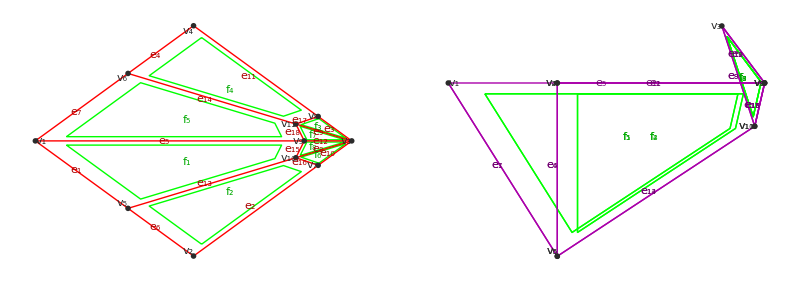

-Graphics-

Fold the neck and head together.

```mathematica
Module[{stobj},
stobj=MakeSplitGraph2D[foo,{{1.1,0},.2U[70.°]}];
GraphicsRow[{SplitGraphGraphics[stobj],SplitGraph2DGraphics[stobj]}]//Print;
foo=SplitAndFoldSplitGraph2D[stobj,{3,8,11,9,10,7}];
GraphicsRow[{GraphGraphics[foo],Graph2DGraphics[foo]}]
]//ShowExample
```

Rotate the folded form.

```mathematica
Module[{},
foo=RotateGraph2D[foo,-22.5°];
GraphicsRow[{GraphGraphics[foo],Graph2DGraphics[foo]}]
]//ShowExample
```

#### DuckGraph2D

DuckGraph2D is a TGraph2D that represents a simple duck; probably the simplest figurate origami example.

```mathematica
Clear[DuckGraph2D];
AddTGraphExample[DuckGraph2D,Module[{verts,edges,tobj,stobj},
(* a square in diamond orientation *)
verts={{0,0},{1,-1},{2,0},{1,1}}//N;
edges={{1,2},{2,3},{3,4},{4,1}};
tobj=MakeTGraph2D[verts,edges]//AddTPlaneGraph;
(* fold in half along horizontal diagonal *)
stobj=MakeSplitGraph2D[tobj,{{0,0},{1,0}}];
tobj=SplitAndFoldSplitGraph2D[stobj,{4}];
(* kite-fold both bottom corners *)
stobj=MakeSplitGraph2D[tobj,{{2,0},.2U[22.5°]}];
tobj=SplitAndFoldSplitGraph2D[stobj,{2,4}];
(* fold the head *)
stobj=MakeSplitGraph2D[tobj,{{1.7,0},.2U[70.°]}];
tobj=SplitAndFoldSplitGraph2D[stobj,{3}];
(* fold the body and head together *)
stobj=MakeSplitGraph2D[tobj,{{1.1,0},.2U[70.°]}];
tobj=SplitAndFoldSplitGraph2D[stobj,{3,8,11,9,10,7}];
(* rotate the folded form *)
RotateGraph2D[tobj,-22.5°]]];
```

Example

```mathematica
Module[{tobj},
tobj=DuckGraph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

#### CraneGraph2D

CraneGraph2D gives the fold pattern for an origami crane, constructed via sequential folding from a Bird BaseGraph2D.

```mathematica
Clear[CraneGraph2D];
AddTGraphExample[CraneGraph2D,Module[{tobj,stobj},
tobj=BirdBaseGraph2D;
(* fold left edge in to the center *)
stobj=MakeSplitGraph2D[tobj,{{0,0},U[101.25°]}];
tobj=SplitAndFoldSplitGraph2D[stobj,{4,6}];
(* fold right edge in to the center *)
stobj=MakeSplitGraph2D[tobj,{{0,0},U[78.75°]}];
tobj=SplitAndFoldSplitGraph2D[stobj,{8,10}];
(* fold up left flap *)
stobj=MakeSplitGraph2D[tobj,{{0,.5},.3U[202.5°]}];
tobj=SplitAndFoldSplitGraph2D[stobj,{1}];
(* fold up right flap *)
stobj=MakeSplitGraph2D[tobj,{{0,.5},.3U[-22.5°]}];
tobj=SplitAndFoldSplitGraph2D[stobj,{13}];
(* fold down head. Note that we have filter the split to fold head but not wings. *)
stobj=MakeSplitGraph2D[tobj,{{0,.73},.5U[0°]}];
GraphicsRow[{SplitGraphGraphics[stobj],SplitGraph2DGraphics[stobj,Frame->True]}]//Hold;
stobj=FilterSplitGraph2D[stobj,{},{22,91,56,96,29,92,58,95}];
SplitAndFoldSplitGraph2D[stobj,{13}]]];
```

Example

```mathematica
Module[{tobj},
tobj=CraneGraph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

## 3D folded forms

#### Notes

We can represent a plane graph as a 3D surface by using 3D Vertices for the embedding. It’s obviously no longer a plane graph if its embedding is 3D, but we’ll keep the terminology, calling it a “3D plane graph.” Once we have a 3D embedding, we also can define fold angles for the edges that take on analog value between -π (fully folded mountain fold) and +π (fully folded valley fold). We introduce a new class, TGraph3D, and two new properties, Vertices3D and FoldAngles, to capture this information.

For objects whose folded form is 3D, a TGraph+TGraph3D can capture both the crease pattern (via Vertices) and the folded form (Vertices3D and FoldAngles), in the same way that a TGraph+TGraph2D captures both crease pattern (via Vertices) and folded form (via Vertices2D).

There is an implicit assumption in this section that the individual faces are planar in their 3D. If they’re not, then computed results will likely be invalid.

### Class TGraph3D

#### TObj class: TGraph3D Mixin with: TGraph or subclass

TGraph3D is a mixin class that can be used to make any TGraph (or subclass of a a TGraph) a 3D embedded graph.

Note that it’s possible for a TObj to inherit from both TGraph2D and TGraph3D. This can be useful for using the 3D embedding to represent the partially-folded state and the 2D embedding to represent the fully-folded state. (The original TGraph embedding represents the unfolded state.)

```mathematica
TGraph3D::usage="TGraph3D is a TObj class that describes a graph with a 3D embedding.";
```

```mathematica
RegisterTClass[TGraph3D,{TGraph}];
```

#### TGraph3D properties: Vertices3D FoldAngles

Vertices3D is a property that gives the 3D embedding of the vertices of a TGraph.

```mathematica
Vertices3D::usage="Vertices3D is a TObj property that specifies a 3D embedding of the vertices of a graph.";
```

FoldAngles is a list of the fold angles for each edge of the TGraph3D. By convention, border edges are assigned a fold angle of 0.

```mathematica
FoldAngles::usage="FoldAngles is a TObj property that specifies the angles of the folds for each edge of a TGraph3D.";
```

#### AddTGraph3DTo[tobj] AddTGraph3DTo[tobj, verts3d] AddTGraph3DTo[tobj, verts3d, foldangles] AddTGraph3D[] AddTGraph3D[verts3d] AddTGraph3D[verts3d, foldangles] MakeTGraph3D[verts, edges, faces] MakeTGraph3D[verts, edges, faces, verts3d] MakeTGraph3D[verts, edges, faces, verts3d, foldangles]

AddTGraph3DTo[tobj] takes a TGraph and sets its Vertices3D to have x- and y-coordinates taken from Vertices and z-coordinate 0 and all FoldAngles set to 0.

AddTGraph3DTo[tobj, verts3d] takes a TGraph and returns a TGraph3D using the specified 3D embedding verts3d and calculates the appropriate FoldAngles.

AddTGraph3DTo[tobj, verts3d, foldangles] takes a TGraph and returns a TGraph3D using the specified 3D embedding verts3d and fold angles foldangles. Note that there is no consistency check, so you can supply inconsistent values in the constructor.

If you want consistency between verts3d and foldangles but only have values for one of them,
	If you have only verts3d, use RecalcFoldAngles, below.
	If you have only foldangles, use FoldGraph3D, below.

```mathematica
AddTGraph3DTo[tobj_TObj,verts3d_List:{}, foldangles_List:{}]:=Module[{v3d,fa,tobj1},
AssertClass[tobj,TGraph,AddTGraph3DTo];
v3d=If[verts3d==={},Append[#,0]&/@GetValue[tobj,Vertices],verts3d];
fa=If[foldangles==={},Table[0,{Length[GetValue[tobj,Edges]]}],foldangles];
AddClassTo[tobj,TGraph3D,{Vertices3D->v3d,FoldAngles->fa}]]
```

Example

```mathematica
Module[{verts,edges,tobj,tobj1},
verts={{0,0},{1,0},{.5,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
tobj=AddTGraph3DTo[tobj];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

AddTGraph3D[verts3d, foldangles] returns a pure function that makes adds the TGraph3D class with property values verts3d and foldangles. Both are optional, so one can use AddTGraph3D[verts3d] (which will calculate the fold angles) or AddTGraph3D[] (which will use the unfolded embedding). If you want to supply foldangles but not verts3d, see FoldGraph3D, below.

```mathematica
AddTGraph3D[verts3d_List:{},foldangles_List:{}]:= AddTGraph3DTo[#,verts3d,foldangles]&
```

Note that when chaining this constructor, you must call the function, even if you’re relying on the default empty list, i.e., do this:
	tobj // AddTGraph3D[]
not this:
	tobj // AddTGraph3D
Most of the time, though, you will have 3D vertex data and so will do this:
	tobj // AddTGraph3D[verts3d]
or this
	tobj // AddTGraph3D[verts3d, foldangles]

MakeTGraph3D[verts, edges, faces, verts3d, foldangles] creates a TGraph3D from parameters.

```mathematica
MakeTGraph3D[verts_List,edges_List,faces_List,verts3d_List:{}, foldangles_List:{}]:=MakeTGraph[verts,edges,faces]//AddTGraph3D[verts3d,foldangles]
```

### TGraph3D rendering

#### FoldAngleForm FoldAngleDigits

FoldAngleForm is an option to FoldAngleLabels that specifies the formatter to use for angles. Some useful examples:
	FoldAngleForm → Round — rounds to integer degrees.
	FoldAngleForm → FoldAngleDigits[n] — display all angles numerically to n decimal places.

```mathematica
FoldAngleForm::usage="FoldAngleForm is an option to FoldAngleLabels that specifies the printed form of the fold angle.";
```

FoldAngleDigits[n] is a number function that displays angles with n digits beyond the decimal point.

The use of Round ensures that super-tiny numbers won’t default to scientific notation.

```mathematica
FoldAngleDigits[n_:0]:=If[n==0,Round,NumberForm[N[Round[# 10^n] 10^-n],{5,n}]&]
```

Example.

```mathematica
Table[FoldAngleDigits[n][π/100],{n,0,3}]//ColumnForm//ShowExample
```

```mathematica
Table[FoldAngleDigits[n][π],{n,0,3}]//ColumnForm//ShowExample
```

```mathematica
Table[FoldAngleDigits[n][100π],{n,0,3}]//ColumnForm//ShowExample
```

#### FoldAngleLabels[tobj, opts] (unchecked class) TGraph3D (options) EdgeIndices, UseDegrees, FoldAngleForm

FoldAngleLabels[tobj, opts] returns a list of labels on the edges of tobj with the label given by its FoldAngles property. Options are:
	EdgeIndices → True | False, specifies whether to display the index of the edge.
	UseDegrees → True | False, specifies whether to show the angles in degrees rather than radians.
	FoldAngleForm → f, where f formats the value of the angle.

```mathematica
EdgeIndices::usage="EdgeIndices is an option to FoldAngleLabels that specifies whether to show the index of the edge.";
```

```mathematica
UseDegrees::usage="UseDegrees is an option to FoldAngleLabels that specifies whether to display angles in degrees.";
```

```mathematica
Options[FoldAngleLabels]={
EdgeIndices->False,
UseDegrees->True,
FoldAngleForm->(#&)
};
```

```mathematica
FoldAngleLabels[tobj_TObj, opts___]:=Module[{ei,ud,faf,verts,edges,foldangles,fa},
ei=EdgeIndices/.{opts}/.Options[FoldAngleLabels];
ud=UseDegrees/.{opts}/.Options[FoldAngleLabels];
faf=FoldAngleForm/.{opts}/.Options[FoldAngleLabels];
{verts,edges,foldangles}=GetValues[tobj,{Vertices,Edges,FoldAngles}];
Table[
fa=foldangles⟦i⟧;
Text[If[ei,"e"<>ToString[i]<>"→",""]<>If[ud,ToString[faf[fa/°]]<>"°",ToString[faf[fa⟦i⟧]]],Plus@@verts⟦edges⟦i⟧⟧/2]
,{i,Length[edges]}]]
```

Example

```mathematica
Module[{verts,edges,tobj,foldangles,edgelabels},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
foldangles={90 °,-90 °,90 °,150 °,90 °,-90 °,90 °,0,0,0,0,0,0};
tobj=MakeTGraph[verts,edges]//AddTGraph3D[{},foldangles];
edgelabels=FoldAngleLabels[tobj,EdgeIndices->True];
GraphGraphics[tobj,EdgeLabels->edgelabels]
]//ShowExample
```

Same thing, but no edge indices and give angles to 2 digits precision.

```mathematica
Module[{verts,edges,tobj,foldangles,edgelabels},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
foldangles={90 °,-90 °,90 °,150 °,90 °,-90 °,90 °,0,0,0,0,0,0};
tobj=MakeTGraph[verts,edges]//AddTGraph3D[{},foldangles];
edgelabels=FoldAngleLabels[tobj,FoldAngleForm->FoldAngleDigits[2]];
GraphGraphics[tobj,EdgeLabels->edgelabels]
]//ShowExample
```

#### FoldAngleGraphics[tobj, opts] (checked classes) TGraph, TGraph3D (options) EdgeIndices, UseDegrees, FoldAngleForm

FoldAngleGraphics[tobj, opts] returns a Graphics object that displays the graph with edges labeled by its FoldAngles. Options are:
	EdgeIndices → True | False, specifies whether to display the index of the edge.
	UseDegrees → True | False, specifies whether to show the angles in degrees rather than radians.
	FoldAngleForm → f, where f formats the value of the angle.

```mathematica
FoldAngleGraphics[tobj_TObj, opts___]:=Module[{elabels},
AssertClass[tobj,TGraph,FoldAngleGraphics];
AssertClass[tobj,TGraph3D,FoldAngleGraphics];
elabels=FoldAngleLabels[tobj,opts];
GraphGraphics[tobj,EdgeLabels->elabels,Faces->False]]
```

Example

```mathematica
Module[{verts,edges,foldangles,tobj},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
foldangles={90 °,-90 °,90 °,150 °,90 °,-90 °,90 °,0,0,0,0,0,0};
tobj=MakeTGraph3D[verts,edges,{},{},foldangles];
FoldAngleGraphics[tobj]
]//ShowExample
```

Example: include edge indices

```mathematica
Module[{verts,edges,foldangles,tobj},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
foldangles={90 °,-90 °,90 °,150 °,90 °,-90 °,90 °,0,0,0,0,0,0};
tobj=MakeTGraph3D[verts,edges,{},{},foldangles];
FoldAngleGraphics[tobj,EdgeIndices->True]
]//ShowExample
```

#### Graph3DGraphics3D[tobj, opts] (checked classes) TGraph, TGraph3D (options) VertexLabels, EdgeLabels, DirectedEdges, VertexColor, EdgeColor, FaceColor, FaceColoring, Options[Graphics3D]

Graph3DGraphics3D[tobj, opts] draws the graph in the same way as GraphGraphics, but tobj should be a TGraph3D, and it returns a Graphics3D object. Options are:
	VertexLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith vertex.
	EdgeLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith edge.
	FaceLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith face.
	DirectedEdges → True | False, display edges as directed edges.
	DirectedEdges3D → True | False, display edges as directed edges using 3D arrows and tubes for lines.
	VertexColor → color, specify the base color for vertices.
	EdgeColor → color, specify the base color for edges.
	FaceColor → color, specify the base color for faces.
	FaceColoring → None | {fc_1, fc_2, ...}, color the faces, where fc_i is ±1. None implies no face coloring.
	Options[Graphics3D]

The default color scheme of Graph3DGraphics3D matches that of Graph2DGraphics, since both are typically used to render the folded form.

```mathematica
DirectedEdges3D::usage="DirectedEdges3D is an option to Graph3DGraphics3D that specifies whether to use 3D arrows for directed edges.";
```

```mathematica
Options[Graph3DGraphics3D]={
VertexLabels->Automatic,
EdgeLabels->Automatic,
FaceLabels->Automatic,
DirectedEdges->False,
DirectedEdges3D->False,
VertexColor->DarkGray,
EdgeColor->Darker[Magenta],
FaceColor->Green,
FaceColoring->None
};
```

```mathematica
Graph3DGraphics3D[tobj_TObj,opts___]:=Module[{vl,el,fl,de,de3d,vc,ec,fc,fcng,verts3d, edges, faces,hf,gg},
vl=VertexLabels/.{opts}/.Options[Graph3DGraphics3D];
el=EdgeLabels/.{opts}/.Options[Graph3DGraphics3D];
fl=FaceLabels/.{opts}/.Options[Graph3DGraphics3D];
de=DirectedEdges/.{opts}/.Options[Graph3DGraphics3D];
de3d=DirectedEdges3D/.{opts}/.Options[Graph3DGraphics3D];
vc=VertexColor/.{opts}/.Options[Graph3DGraphics3D];
ec=EdgeColor/.{opts}/.Options[Graph3DGraphics3D];
fc=FaceColor/.{opts}/.Options[Graph3DGraphics3D];
fcng=FaceColoring/.{opts}/.Options[Graph3DGraphics3D];
AssertClass[tobj,TGraph,Graph3DGraphics3D];
AssertClass[tobj,TGraph3D,Graph3DGraphics3D];
{verts3d, edges, faces} = GetValues[tobj,{Vertices3D, Edges, Faces}];
hf = HasFacesQ[tobj];
gg = {};
If[hf,
If[!(fcng===None),AppendTo[gg,MapThread[Style[Polygon[verts3d⟦#1⟧],Lighter[fc,.8-.1#2]]&,{faces,fcng}]]];
AppendTo[gg,Style[PolyLines[verts3d,faces],fc]];
];
Which[
de,AppendTo[gg,Style[DirectedEdgeLines[verts3d,edges],ec]],
de3d,AppendTo[gg,Style[DirectedEdgeLines3D[verts3d,edges],ec]],
True,AppendTo[gg,Style[EdgeLines[verts3d,edges],ec]]];
If[hf,AppendTo[gg,Style[Switch[fl,None,{},Automatic,StdFaceLabels[verts3d,faces],_,fl],Darker[fc,0.75]]]];
AppendTo[gg,Style[Switch[el,None,{},Automatic,StdEdgeLabels[verts3d,edges],_,el],Darker[ec,0.75]]];
AppendTo[gg,Style[Switch[vl,None,{},Automatic,StdVertexLabels[verts3d],_,vl],vc,AbsolutePointSize[4]]];
Graphics3D[gg,FilterRules[{opts},Options[Graphics3D]]]]
```

Example. 3D, no faces.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
tobj=MakeTGraph3D[verts,edges,{}];
Graph3DGraphics3D[tobj,Boxed->True]
]
```

-Graphics3D-

Example. 3D, with faces, also use 3D arrows.

```mathematica
Module[{verts,edges,faces,tobj,fc},
verts={{0,0},{1,0},{1,.5},{0,.5}};
edges={{1,2},{2,3},{3,4},{4,1},{1,3}};
faces={{1,2,3},{1,3,4}};
tobj=MakeTGraph3D[verts,edges,faces];
Graph3DGraphics3D[tobj,DirectedEdges3D->True,FaceColoring->{1,-1},Boxed->True]
]
```

-Graphics3D-

### Solving for developable 3D fold angles

#### Notes

When we take a TGraph into 3D, its folds are no longer simple Mountain, Valley, or Unfolded; they can take on arbitrary angular values between -π and π. The fold angles canot be chosen arbitrarily; in order to satisfy developability, they need to satisfy the generalized Kawasaki condition at each interior vertex. The functions in this section provide the ability to solve for self-consistent sets of fold angles for a TGraph.

#### FoldAngleSpecLabels[tobj, faspecs, opts] (checked class) TGraph (options) EdgeIndices, UseDegrees

FoldAngleSpecGraphics[tobj, faspecs, opts] returns a Graphics object that displays the graph with edges labeled by the specified fold angle specifications faspecs, which are a list of the form {{w_i,α_i}, ...}, where w_i is a weight for the ith edge and α_i is the associated fold angle. Options are:
	EdgeIndices → True | False, specifies whether to display the index of the edge on top of the edge.
	UseDegrees → True | False, specifies whether to show the angles in degrees rather than radians.

```mathematica
Options[FoldAngleSpecLabels]={
EdgeIndices->False,
UseDegrees->True
};
```

```mathematica
FoldAngleSpecLabels[tobj_TObj, faspecs_List, opts___]:=Module[{ei,ud,verts,edges,el},
ei=EdgeIndices/.{opts}/.Options[FoldAngleLabels];
ud=UseDegrees/.{opts}/.Options[FoldAngleSpecLabels];
AssertClass[tobj,TGraph,FoldAngleSpecLabels];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
Table[Text[If[ei,"e"<>ToString[i]<>"→{","{"]<>ToString[faspecs⟦i,1⟧/.Infinity->"∞"]<>", "<>If[ud,ToString[faspecs⟦i,2⟧/°]<>"°",ToString[faspecs⟦i,2⟧]]<>"}",Plus@@verts⟦edges⟦i⟧⟧/2],{i,Length[edges]}]]
```

Example

```mathematica
Module[{verts,edges,faspecs,tobj,edgelabels},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
tobj=MakeTGraph[verts,edges];
faspecs={{1,90°},{1,-90°},{1,90°},{∞,150°},{1,90°},{1,-90°},{1,90°},{∞,0},{∞,0},{∞,0},{∞,0},{∞,0},{∞,0}};
edgelabels=FoldAngleSpecLabels[tobj,faspecs];
GraphGraphics[tobj,EdgeLabels->edgelabels,Faces->False]
]//ShowExample
```

#### FoldAngleSpecGraphics[tobj, faspecs, opts] (checked class) TGraph (options) EdgeIndices, UseDegrees

FoldAngleSpecGraphics[tobj, faspecs, opts] returns a Graphics object that displays the graph with edges labeled by the specified fold angle specifications faspecs, which are a list of the form {{w_i,α_i}, ...}, where w_i is a weight for the ith edge and α_i is the associated fold angle. Options are:
	EdgeIndices → True | False, specifies whether to display the index of the edge on top of the edge.
	UseDegrees → True | False, specifies whether to show the angles in degrees rather than radians.

```mathematica
FoldAngleSpecGraphics[tobj_TObj, faspecs_List, opts___]:=GraphGraphics[tobj,EdgeLabels->FoldAngleSpecLabels[tobj,faspecs,opts],Faces->False]
```

Example

```mathematica
Module[{verts,edges,faspecs,tobj},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
tobj=MakeTGraph[verts,edges];
faspecs={{1,90°},{1,-90°},{1,90°},{∞,150°},{1,90°},{1,-90°},{1,90°},{∞,0},{∞,0},{∞,0},{∞,0},{∞,0},{∞,0}};
FoldAngleSpecGraphics[tobj,faspecs]
]//ShowExample
```

#### MakeGraphFoldAngles[tobj, faspecs, opts] (checked classes) TGraph (options) ConstrainFoldDirection

MakeGraphFoldAngles[tobj, faspecs, opts] takes a TGraph tobj and a set of fold angle specifications faspecs and solves for a self-consistent set of edge angles that satisfies the generalized Kawasaki loop consistency condition at each interior vertex. faspecs is a list of the form {{w_1,α_1},...} with an entry for each edge of the graph. w_i is a weight that determines the type of constraint on the ith angle and α_i is a target value for that angle. The behavior varies according to the weight:
	w_i=0 specifies a free angle (can take on any value to satisify GKC, and α_i is taken as the initial value in the search.
	w_i∈(0,∞) specifies a goal angle, for which we minimize the RMS deviation from α_i and use weighting value w_i in the sum-of-squared-error.
	w_i=∞ specifies a fixed constraint, where we set the angle to this value.
There must be an entry for each edge in the pattern, but B edges will have their edge angles set to zero no matter what the spec said.
The return value is a list foldangles, which can be fed to FoldGraph3D to generate a 3D folded form. Note that for this function, tobj does not need to be a TGraph3D, but FoldGraph3D requires it. Options are:
	ConstrainFoldDirection → True | False. If True, the fold angles with finite weight are forced to have their mountain-valley status match the angle sign in the spec. If the spec angle is 0 but the angle is free or goal, then there is no constraint placed on the angle.

```mathematica
ConstrainFoldDirection::usage="ConstrainFoldDirection is an option to MakeGraphFoldAngles that specifies whether to bound the direction of the creases.";
```

```mathematica
Options[MakeGraphFoldAngles]={
ConstrainFoldDirection->True
};
```

```mathematica
MakeGraphFoldAngles[tobj_TObj, faspecs_List,opts___]:=Module[{bfd,tobj1,faspecs1,iverts,bedges,vei,vars,angles,a,vea,vfa,krms,fom,kcons,bcons,val,soln},
bfd=ConstrainFoldDirection/.{opts}/.Options[MakeGraphFoldAngles];
tobj1=tobj;(* make a copy to work on *)
If[!HasClassQ[tobj1,TPlaneGraph],tobj1=tobj1//RebuildPlaneGraph];
faspecs1=faspecs; (* ditto *)
{iverts,bedges,vei}=GetValues[tobj1,{InteriorVertices,BoundaryEdges,VertexEdgeIncidence}];
(* groom the specs by setting all boundary edges to {0,0} *)
(faspecs1⟦#⟧={∞,0})&/@bedges;
(* make lists of variables and angles (either as variable a[i] or value) *)
vars={};
angles=Table[If[faspecs1⟦i,1⟧==∞,faspecs1⟦i,2⟧,AppendTo[vars,{a[i],faspecs1⟦i,2⟧}];a[i]],{i,Length[faspecs1]}];
vea=angles⟦#⟧&/@vei;(* dihedral angles around each vertex *)
vfa=VertexEdgeAngles[tobj1];(* sector angles around each vertex *)
(* generalized Kawasaki condition matrices on each interior vertex *)
krms=Table[VertexConsistencyMatrix3D[vea⟦iverts⟦i⟧⟧,vfa⟦iverts⟦i⟧⟧],{i,Length[iverts]}];
kcons=And@@Flatten[{#⟦1,2⟧==0,#⟦1,3⟧==0,#⟦2,3⟧==0,#⟦1,1⟧>0,#⟦2,2⟧>0,#⟦3,3⟧>0}&/@krms];
(* figure of merit on goal vertices *)
fom=Plus@@Table[Switch[faspecs1⟦i,1⟧,0,0,∞,0,_,faspecs1⟦i,1⟧(a[i]-faspecs1⟦i,2⟧)^2],{i,Length[faspecs1]}];
(* bounds on angle variables *)
bcons=And@@If[bfd,
#⟦1⟧≤(If[#⟦2⟧<0,0,π])&&#⟦1⟧≥(If[#⟦2⟧>0,0,-π])&/@vars,
#⟦1⟧≤π&&#⟦1⟧≥-π&/@vars];
(* solve for all unknown angles *)
{val,soln}=FindMinimum[{fom,kcons&&bcons},vars];
angles/.soln
]
```

Example

```mathematica
Module[{verts,edges,tobj,faspecs,gmj,gmn,foldangles,tobj1},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
tobj=MakeTGraph[verts,edges];
faspecs={{1,90 °},{1,-90 °},{1,90 °},{1,90 °},{1,90 °},{1,-90 °},{1,90 °},{∞,0},{∞,0},{∞,0},{∞,0},{∞,0},{∞,0}};
faspecs⟦4⟧={∞,100.°};(* fix one angle *)
foldangles=MakeGraphFoldAngles[tobj,faspecs];(* solve for remaining angles *)
Print[FoldAngleSpecGraphics[tobj,faspecs]];
foldangles/°
]//ShowExample
```

### TGraph3D interrogators

#### EdgeLengths3D[tobj] (unchecked class) TGraph3D

EdgeLengths3D[tobj] returns a list of the lengths of the edges, in the same order as Edges.

```mathematica
EdgeLengths3D[tobj_TObj]:=Module[{verts3d,edges},
{verts3d,edges}=GetValues[tobj,{Vertices3D,Edges}];
Mag[Subtract@@verts3d⟦#⟧]&/@edges]
```

#### FaceCentroids3D[tobj] (unchecked class) TGraph3D

FaceCentroids[tobj] takes a TGraph3D and constructs the 3D centroids of the faces.

```mathematica
FaceCentroids3D[tobj_TObj]:=Module[{verts3d,faces},
{verts3d,faces}=GetValues[tobj,{Vertices3D,Faces}];
FaceCentroid[verts3d,#]&/@faces
]
```

#### FaceNormal3D[verts3d, face]

FaceNormal3D[verts3d, face] returns the face normal vector for a CCW face on a 3D vertex embedding.

```mathematica
FaceNormal3D[verts3d_List,face_List]:=Module[{c},
c=FaceCentroid[verts3d,face];
NormalizeReal[(verts3d⟦face⟦1⟧⟧-c)×(verts3d⟦face⟦2⟧⟧-c)]]
```

Example

```mathematica
Module[{verts3d,face},
verts3d={{0,0,0},{1,0,0},{1,1,0},{0,1,0}};
face={1,2,3,4};
FaceNormal3D[verts3d,face]
]//ShowExample
```

#### FaceNormals3D[tobj] (unchecked class) TGraph3D

FaceNormals3D[tobj] takes a TGraph3D representing a 3D graph and returns a list of vectors that are the face normal vectors in 3D, oriented to point towards the white side of the paper.

```mathematica
FaceNormals3D[tobj_TObj]:=Module[{verts3d,faces,fc},
{verts3d,faces}=GetValues[tobj,{Vertices3D,Faces}];
fc=FaceCentroids3D[tobj];
MapThread[NormalizeReal[(verts3d⟦#1⟦1⟧⟧-#2)×(verts3d⟦#1⟦2⟧⟧-#2)]&,{faces,fc}]]
```

Example: a valley fold.

```mathematica
Module[{verts,edges,faces,tobj,verts3d},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1},{2,0,0},{2,1,0},{1,1,-1},{0,1,0}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d];
Print[Graph3DGraphics3D[tobj]];
FaceNormals3D[tobj]
]//ShowExample
```

### TGraph3D+TPlaneGraph interrogators

#### EdgeFaceAngles3D[tobj] (unchecked classes) TGraph3D, TPlaneGraph

EdgeFaceAngles3D[tobj] takes a TObj representing a 3D plane graph and computes a list {γ_1, γ_2, ...} of the dihedral (fold) angles on each edge of the graph. Border edges are assigned a fold angle of 0. Note that badness will happen if any two faces incident to the same edge are parallel.

Note: this is the FoldAngles property of a TGraph3D. Use this function if you’ve altered the Vertices3D property (and you should probably update the FoldAngles property with the results of this). Alternatively, you can use the result of this as a check on the consistency of FoldAngles property. We use this function to recalculate the fold angles, see RecalcFoldAngles, below.

New version

```mathematica
EdgeFaceAngles3D[tobj_TObj]:=Module[{verts3d,edges,faces,efi,fc,fn,ei,fi},
{verts3d,edges,faces,efi}=GetValues[tobj,{Vertices3D,Edges,Faces,EdgeFaceIncidence}];
fc=FaceCentroids3D[tobj];
fn=FaceNormals3D[tobj];
Table[
ei=edges⟦i⟧;(* each edge as vertex index pair *)
fi=efi⟦i⟧;(* faces incident to the edge as face indices *)
If[MemberQ[fi,0],
0,(* is boundary edge, return 0, else: *)
DirectedAngle3D[fn⟦fi⟦1⟧⟧,fn⟦fi⟦2⟧⟧,verts3d⟦ei⟦2⟧⟧-verts3d⟦ei⟦1⟧⟧] ],
{i,Length[edges]}]
]
```

Example: a valley fold.

```mathematica
Module[{verts,edges,faces,tobj,verts3d},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1},{2,0,0},{2,1,0},{1,1,-1},{0,1,0}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d];
Print[Graph3DGraphics3D[tobj]];
EdgeFaceAngles3D[tobj]
]//ShowExample
```

Example: a mountain fold.

```mathematica
Module[{verts,edges,faces,tobj,verts3d},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,1},{2,0,0},{2,1,0},{1,1,1},{0,1,0}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d];
Print[Graph3DGraphics3D[tobj]];
EdgeFaceAngles3D[tobj]
]//ShowExample
```

#### VertexEdgeAngles3D[tobj] (unchecked classes) TGraph3D, TPlaneGraph

VertexEdgeAngles3D[tobj] takes a TObj representing a 3D plane graph and returns a list {{α_1, α_2, ...}, ...} of the sector angles around each vertex where each list {α_1, α_2, ...} is a list of the sector angles around the corresponding vertex. Exterior angles are given as Null since there is no reference plane for any exterior angle in 3D. The list is ordered to correspond to propertyVertexFaceIncidences, i.e., an angle in VertexEdgeAngles3D is at the same position as its corresponding face in VertexFaceIncidence.

As with VertexEdgeAngles2D, a good check of the consistency of the folded form is to see if VertexEdgeAngles and VertexEdgeAngles3D return the same values.

```mathematica
VertexEdgeAngles3D[tobj_TObj]:=Module[{verts3d,vva,vfi,fn,vc,va,vf},
{verts3d,vva,vfi}=GetValues[tobj,{Vertices3D,VertexVertexAdjacency,VertexFaceIncidence}];
fn=FaceNormals3D[tobj];
Table[
vc=verts3d⟦i⟧;(* this vertex coords *)
va=vva⟦i⟧;(* vertices adjacent to this vertex, by index *)
vf=vfi⟦i⟧;(* faces incident to this vertex, by index. Could include zeroes. *)
Table[
If[vf⟦j⟧==0,
Null,
DirectedAngle3D[verts3d⟦va⟦j⟧⟧-vc,verts3d⟦va⟦Mod[j+1,Length[va],1]⟧⟧-vc,fn⟦vf⟦j⟧⟧]
],{j,Length[va]}]
,{i,Length[verts3d]}]]
```

Example: 3D valley fold.

```mathematica
Module[{verts,edges,faces,tobj,verts3d},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d];
Print[Graph3DGraphics3D[tobj]];
VertexEdgeAngles3D[tobj]
]//ShowExample
```

Example: Compare crease pattern and folded form.

```mathematica
Module[{verts,edges,faces,tobj,verts3d},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d];
Print[Graph3DGraphics3D[tobj]];
Chop[N[VertexEdgeAngles3D[tobj]-VertexEdgeAngles[tobj]]]
]//ShowExample
```

#### SingleVertexEdgeAngles3D[tobj, i0, i1] (unchecked classes) TGraph3D, TPlaneGraph

SingleVertexEdgeAngles3D[tobj, i0, i1] returns the face angles around vertex i0 oriented so that the first angle is the face that follows edge {i0, i1}.

```mathematica
SingleVertexEdgeAngles3D::badedge="Vertex `1` is not adjacent to vertex `2`.";
```

```mathematica
SingleVertexEdgeAngles3D[tobj_TObj, i0_, i1_]:=Module[{verts3d,vva,vfi,fn,vc,va,vf,vfa},
{verts3d,vva,vfi}=GetValues[tobj,{Vertices3D,VertexVertexAdjacency,VertexFaceIncidence}];
fn=FaceNormals3D[tobj];
vc=verts3d⟦i0⟧;(* this vertex coords *)
va=vva⟦i0⟧;(* vertices adjacent to this vertex, by index *)
If[!MemberQ[va,i1],Message[SingleVertexEdgeAngles3D::badedge,i1,i0];Abort[]];
vf=vfi⟦i0⟧;(* faces incident to this vertex, by index. Could include zeroes. *)
vfa=Table[
If[vf⟦j⟧==0,
Null,
DirectedAngle3D[verts3d⟦va⟦j⟧⟧-vc,verts3d⟦va⟦Mod[j+1,Length[va],1]⟧⟧-vc,fn⟦vf⟦j⟧⟧]
],{j,Length[va]}];
RotateLeft[vfa,Position[va,i1,1,1]⟦1,1⟧-1]]
```

Example: 3D valley fold.

```mathematica
Module[{verts,edges,faces,tobj,verts3d},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d];
Print[Graph3DGraphics3D[tobj]];
SingleVertexEdgeAngles3D[tobj,2,3]
]//ShowExample
```

#### EdgeVertexAngles3D[tobj] (unchecked class) TGraph3D, TPlaneGraph

EdgeVertexAngles[tobj] returns a list of the four sector angles around both vertices of all of the edges, of the form {{{α_(i,r), α_(i,l)},{α_(j,r),α_(j,l)}}, …}, where each list {{α_(i,r), α_(i,l)},{α_(j,r),α_(j,l)}} applies to edge {i,j} of tobj, and angle α_(i,r) lies to the right of vertex i, as viewed from the edge, α_(i,l) lies to its left, and similarly for the other two angles. Or, equivalently, for each edge, the first angle lies CCW of the first vertex, and then the angles circulate CCW about the edge. Same as EdgeVertexAngles, but computed from the Vertices3D data.

```mathematica
EdgeVertexAngles3D[tobj_TObj]:=Module[{edges,vei,vea,ia,ib,veaa,veab},
{edges,vei}=GetValues[tobj,{Edges,VertexEdgeIncidence}];
vea=VertexEdgeAngles3D[tobj];
Table[
{ia,ib}=edges⟦i⟧;
veaa=RotateLeft[vea⟦ia⟧,Position[vei⟦ia⟧,i]⟦1,1⟧-1];(* edge angles around vertex ia *)
veab=RotateLeft[vea⟦ib⟧,Position[vei⟦ib⟧,i]⟦1,1⟧-1];(* edge angles around vertex ib *)
{{veaa⟦1⟧,veaa⟦-1⟧},{veab⟦1⟧,veab⟦-1⟧}}
,{i,Length[edges]}]]
```

Example: 3D valley fold.

```mathematica
Module[{verts,edges,faces,tobj,verts3d},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d];
Print[GraphicsRow[{GraphGraphics[tobj],Graph3DGraphics3D[tobj]}]];
Print[edges];
EdgeVertexAngles[tobj]
]//ShowExample
```

### 3D-folding and unfolding

#### RecalcFoldAngles[tobj] (checked class) TGraph3D

RecalcFoldAngles[tobj] computes the fold angles from the current 3D embedding and reassigns the FoldAngles property.

Note: if you’re calculating fold angles and there are ±180° folds in the enbedding, then there could be sign errors in the fold angle, since there’s no local way locally to unambiguously determine the parity of the crease assignment. If we have a crease assignment (as part of a TAssignedGraph, see below), then we can more accurately set the FoldAngles by using the TweakFoldAngles function (below) and the hinting that comes from the EdgeType assignments.

```mathematica
RecalcFoldAngles[tobj_TObj]:=Module[{tobj1,fa},
AssertClass[tobj,TGraph3D,RecalcFoldAngles];
tobj1=If[HasClassQ[tobj,TPlaneGraph],tobj,tobj//RebuildPlaneGraph];
fa=EdgeFaceAngles3D[tobj1];
tobj//ReplaceProperty[FoldAngles->fa]]
```

Example: a simple 3D Z-fold. We provide the embedding initially, then recalculate the fold angles.

```mathematica
Module[{verts,edges,faces,verts3d,tobj},
verts={{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{5,6},{6,7},{7,8},{1,5},{2,6},{3,7},{4,8}};
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7}};
verts3d={{0,0,0},{1,0,0},{1,0,1},{2,0,1},{0,1,0},{1,1,0},{1,1,1},{2,1,1}};
tobj=MakeTGraph3D[verts,edges,faces,verts3d];
tobj=RecalcFoldAngles[tobj];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

#### FoldGraph3D[tobj, foldangles, opts] (checked class) TGraph (options) StationaryFace, ShowProgress

FoldGraph3D[tobj, foldangles, opts] takes a TGraph and a set of fold angles foldangles for each edge, and returns a TGraph3D with a new set of 3D Vertices that specifies the new 3D form according to those fold angles.

Arguments:
	tobj — the TGraph to be folded.
	foldangles — the fold angles.

Options:
	StationaryFace → sface, the index of the face whose position remains unchanged.
	ShowProgress → True | False, whether to show progress and internal structures. Useful for debugging.

Returns a TGraph3D with the 3D folded form.

```mathematica
FoldGraph3D[tobj_TObj,foldangles_List,opts___]:=Module[{verts3d},
AssertClass[tobj,TGraph,FoldGraph3D];
verts3d=FoldEmbedding[tobj,tobj[Vertices],foldangles,opts];
If[HasClassQ[tobj,TGraph3D],tobj//ReplaceProperties[{Vertices3D->verts3d,FoldAngles->foldangles}],tobj//AddTGraph3D[verts3d,foldangles]]]
```

Example: a valley fold. Show all details.

```mathematica
Module[{verts,edges,foldangles,verts3d,tobj,tobj1},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
foldangles={0,90°,0,0,0,0,0};
tobj=MakeTGraph[verts,edges]//AddTGraph3D[verts3d, foldangles]//AddTPlaneGraph;
(* re-fold it to the new angle, keeping original orientation of facet 2 *)
tobj1=FoldGraph3D[tobj,foldangles,StationaryFace->2,ShowProgress->True];
GraphicsRow[{Graph3DGraphics3D[tobj],Graph3DGraphics3D[tobj1]}]
]//ShowExample
```

Same thing, but start from a bare crease pattern. Stationary face will now be in the default position in the x-y plane.

```mathematica
Module[{verts,edges,foldangles,verts3d,tobj,tobj1},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
foldangles={0,90°,0,0,0,0,0};
tobj=MakeTGraph[verts,edges];
(* re-fold it to the new angle, keeping original orientation *)
tobj1=FoldGraph3D[tobj,foldangles,StationaryFace->2,ShowProgress->False];
GraphicsRow[{
GraphGraphics[tobj],
Graph3DGraphics3D[tobj1]
}]
]//ShowExample
```

A single degree-2 vertex.

```mathematica
Module[{verts,edges,tobj,verts3d,foldangles,tobj1},
verts={{0,0},{2,0},{0,1},{1,1},{2,1},{0,2},{2,2}};
edges={{1,2},{1,3},{2,5},{3,4},{4,5},{3,6},{5,7},{6,7}};
tobj=MakeTGraph[verts,edges];
verts3d=Append[#,0]&/@verts;
foldangles={0,0,0,90°,90°,0,0,0};
tobj1=FoldGraph3D[tobj,foldangles,StationaryFace->2,ShowProgress->False];
GraphicsRow[{
GraphGraphics[tobj],
Graph3DGraphics3D[tobj1]
}]]//ShowExample
```

Example. A folded vertex.

```mathematica
Module[{verts,edges,faces,foldangles,tobj},
verts={{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,Tan[30°]},{-1,-1},{-Tan[30°],-1},{1,-1}};
edges={{1,2},{1,4},{1,6},{1,8},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,2}};
faces={{1,2,3,4},{1,4,5,6},{1,6,7,8},{1,8,9,2}};
foldangles={2 ArcTan[1+2/(√3)],-60 °,2 ArcTan[1+2/(√3)],60 °,0,0,0,0,0,0,0,0};
tobj=MakeTGraph[verts,edges,faces]//AddTGraph3D[];
tobj=FoldGraph3D[tobj,foldangles];
GraphicsRow[{
GraphGraphics[tobj],
Graph3DGraphics3D[tobj]
}]]//ShowExample
```

Example: a Miura-ori.

```mathematica
Module[{o,verts,edges,α2,α1,gmj,gmn,foldangles,tobj,tobj1,tobj2},
(* crease pattern *)
o=0.2;(* offset of central row *)
verts={{0,0},{o,1},{0,2},{1,0},{1+o,1},{1,2},{2,0},{2+o,1},{2,2},{3,0},{3+o,1},{3,2}};
edges={{1,2},{2,3},{1,4},{2,5},{3,6},{4,5},{5,6},{4,7},{5,8},{6,9},{7,8},{8,9},{7,10},{8,11},{9,12},{10,11},{11,12}};
(* Get sector angles *)
α1=RotationAngle[verts⟦8⟧-verts⟦5⟧,verts⟦6⟧-verts⟦5⟧];
Print["α_1/° = ",α1/°];
α2=RotationAngle[verts⟦6⟧-verts⟦5⟧,verts⟦2⟧-verts⟦5⟧];
Print["α_2/° = ",α2/°];
(* 2D graph *)
tobj=MakeTGraph[verts,edges,{}]//AddTPlaneGraph;
(* flat 3D form *)
tobj1=tobj//AddTGraph3D[];
(* folded 3D form *)
(* Choose the major fold angle, calculate the minor fold angle *)
gmj=60.°;
Print["γ_major/° = ",gmj/°];
gmn=2 ArcTan[Sin[1/2(α1-α2)]/Sin[1/2(α1+α2)] Tan[gmj/2]];
Print["γ_minor/° = ",gmn/°];
(* Set the edge angles *)
foldangles={0,0,0,-gmn,0,gmj,gmj,0,gmn,0,-gmj,-gmj,0,-gmn,0,0,0};
tobj2=FoldGraph3D[tobj1,foldangles];
GraphicsRow[{GraphGraphics[tobj],Graph3DGraphics3D[tobj1],Graph3DGraphics3D[tobj2]}]
]//ShowExample
```

#### UnfoldGraph3D[tobj] (checked class) TGraph3D (options) StationaryFace, ShowProgress

UnfoldGraph3D[tobj, opts] unfolds a TGraph3D from the Vertices3D embedding in the same way that UnfoldGraphic2D unfolded it from the Vertices2D embedding.

Arguments:
	tobj — the TGraph to be folded.
	foldangles — the fold angles.

Options:
	StationaryFace → sface, the index of the face whose position remains unchanged.
	ShowProgress → True | False, whether to show progress and internal structures. Useful for debugging.

Returns a TGraph3D with the unfolded crease pattern in Vertices. We use a standard position of putting the stationary vertex at the origin and the first edge in that face along the x-axis.

```mathematica
Options[UnfoldGraph3D]={
StationaryFace->1
};
```

```mathematica
UnfoldGraph3D[tobj_TObj,opts___]:=Module[{sface,tobj1,foldangles,verts3d,faces,m,verts},
AssertClass[tobj,TGraph3D,UnfoldGraph3D];
sface=StationaryFace/.{opts}/.Options[UnfoldGraph3D];
tobj1=If[HasClassQ[tobj,TPlaneGraph],tobj,tobj//RebuildPlaneGraph];
{verts3d,faces}=GetValues[tobj1,{Vertices3D,Faces}];
foldangles=-EdgeFaceAngles3D[tobj1];
verts3d=FoldEmbedding[tobj1,verts3d,foldangles,opts];
(* translate to origin *)
verts3d=#-verts3d⟦faces⟦sface,1⟧⟧&/@verts3d;
(* rotate so that stationary face lies in x-y plane with first edge along x-axis. *)
m=TriangleBasis3D@@(verts3d⟦#⟧&/@Take[faces⟦sface⟧,3]);
verts3d=m.#&/@verts3d;
verts=Drop[#,-1]&/@verts3d;
tobj//ReplaceProperty[Vertices->verts]]
```

Example: a valley fold. Fold and then unfold again.

```mathematica
Module[{verts,edges,foldangles,verts3d,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
foldangles={0,90°,0,0,0,0,0};
tobj=MakeTGraph[verts,edges]//AddTGraph3D[verts3d, foldangles]//AddTPlaneGraph;
(* re-fold it to the new angle, keeping original orientation *)
tobj1=FoldGraph3D[tobj,foldangles,StationaryFace->2];
tobj2=UnfoldGraph3D[tobj1,ShowProgress->False];
GraphicsRow[{
GraphGraphics[tobj],
Graph3DGraphics3D[tobj1],
GraphGraphics[tobj2]
}]
]//ShowExample
```

Example. A folded vertex. Fold it up, then unfold it again. Offset and rotate the original vertex to show that unfolding it puts it in a standard position.

```mathematica
Module[{verts,edges,faces,foldangles,tobj,tobj1},
verts={{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,Tan[30°]},{-1,-1},{-Tan[30°],-1},{1,-1}};
verts = {.2,.3}+RotationMatrix2D[10.°].#&/@verts;
edges={{1,2},{1,4},{1,6},{1,8},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,2}};
faces={{1,2,3,4},{1,4,5,6},{1,6,7,8},{1,8,9,2}};
foldangles={2 ArcTan[1+2/(√3)],-60 °,2 ArcTan[1+2/(√3)],60 °,0,0,0,0,0,0,0,0}//N;
tobj=MakeTGraph[verts,edges,faces];
tobj=FoldGraph3D[tobj,foldangles];
tobj1=UnfoldGraph3D[tobj];
GraphicsRow[{
GraphGraphics[tobj,Axes->True],
Graph3DGraphics3D[tobj],
GraphGraphics[tobj1,Axes->True]
}]]//ShowExample
```

### Translation, 3D rotation

#### TranslateGraph3D[tobj, r] (checked class) TGraph3D

TranslateGraph3D[tobj, r] takes a TGraph3D tobj and translates the folded form by the vector r.

```mathematica
TranslateGraph3D[tobj_TObj, r_]:=Module[{verts3d},
AssertClass[tobj,TGraph3D,TranslateGraph3D];
verts3d=GetValue[tobj,Vertices3D];
verts3d=#+r&/@verts3d;
tobj//ReplaceProperty[Vertices3D->verts3d]]
```

Example

```mathematica
Module[{verts,edges,foldangles,verts3d,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
foldangles={0,90°,0,0,0,0,0};
tobj=MakeTGraph[verts,edges];
(* re-fold it to the new angle, keeping original orientation *)
tobj1=FoldGraph3D[tobj,foldangles];
tobj2=TranslateGraph3D[tobj1,{1,1,1}];
GraphicsRow[{
GraphGraphics[tobj],
Graph3DGraphics3D[tobj1,Axes->True,AxesLabel->{"x","y","z"}],
Graph3DGraphics3D[tobj2,Axes->True,AxesLabel->{"x","y","z"}]
}]
]//ShowExample
```

#### RotateGraph3D[tobj, ϕ, w] (checked class) TGraph3D

RotateGraph3D[tobj, {ϕ, w}] takes a TGraph3D tobj and rotates the folded form about the origin through angle ϕ about axis w, which does not need to be normalized.

```mathematica
RotateGraph3D[tobj_TObj, ϕ_, w_]:=Module[{verts3d},
AssertClass[tobj,TGraph3D,RotateGraph3D];
verts3d=GetValue[tobj,Vertices3D];
verts3d=RotationMatrix3D[ϕ,w].#&/@verts3d;
tobj//ReplaceProperty[Vertices3D->verts3d]]
```

Example

```mathematica
Module[{verts,edges,foldangles,verts3d,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
foldangles={0,90°,0,0,0,0,0};
tobj=MakeTGraph[verts,edges];
(* re-fold it to the new angle, keeping original orientation *)
tobj1=FoldGraph3D[tobj,foldangles];
tobj2=RotateGraph3D[tobj1,π/10,{0,1,0}];
GraphicsRow[{
GraphGraphics[tobj],
Graph3DGraphics3D[tobj1,Axes->True,AxesLabel->{"x","y","z"}],
Graph3DGraphics3D[tobj2,Axes->True,AxesLabel->{"x","y","z"}]
}]
]//ShowExample
```

#### VertexRotateGraph3D[tobj, {io, ix, iy}] (checked class) TGraph3D

VertexRotateGraph3D[tobj, {io, ix, iy}] takes a TGraph3D tobj, translates it so that vertex io is at the origin, then rotates its folded form so that vertex ix lies on the positive x-axis and vertex iy lies on the positive y-axis.

This is useful for, among other things, putting planar mechanisms (like Miura-ori) into a standard orientation.

```mathematica
VertexRotateGraph3D::badind="Index specification `1` is invalid because `2` only has `3` vertices.";
```

```mathematica
VertexRotateGraph3D[tobj_TObj, {io_, ix_, iy_}]:=Module[{nv,verts3d},
AssertClass[tobj,TGraph3D,VertexRotateGraph3D];
nv=Length[tobj[Vertices]];
If[io<1||io>nv||ix<1||ix>nv||iy<1||iy>nv,Message[VertexRotateGraph3D::badind,{io,ix,iy},tobj,nv];Abort[]];
verts3d=GetValue[tobj,Vertices3D];
verts3d= #-verts3d⟦io⟧&/@verts3d;
If[Chop[Mag[verts3d⟦ix⟧×{1,0,0}]]≠0,
verts3d=RotationMatrix[{verts3d⟦ix⟧,{1,0,0}}].#&/@verts3d];
If[Chop[Mag[verts3d⟦iy⟧×{0,1,0}]]≠0,
verts3d=RotationMatrix[{verts3d⟦iy⟧,{0,1,0}}].#&/@verts3d];
tobj//ReplaceProperty[Vertices3D->verts3d]]
```

Example

```mathematica
Module[{verts,edges,foldangles,verts3d,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,5},{5,6},{6,1},{2,3},{3,4},{4,5}};
verts3d={{0,0,0},{1,0,-1/2},{2,0,0},{2,1,0},{1,1,-1/2},{0,1,0}};
foldangles={0,90°,0,0,0,0,0};
tobj=MakeTGraph[verts,edges];
(* re-fold it to the new angle, keeping original orientation *)
tobj1=FoldGraph3D[tobj,foldangles];
tobj2=VertexRotateGraph3D[tobj1,{5,4,6}];
GraphicsRow[{
GraphGraphics[tobj],
Graph3DGraphics3D[tobj1,Axes->True,AxesLabel->{"x","y","z"}],
Graph3DGraphics3D[tobj2,Axes->True,AxesLabel->{"x","y","z"}]
}]
]//ShowExample
```

## Primal-dual graphs

### Class TPrimalDualGraph

#### Notes

Many origami tessellation algorithms are based on a primal plane graph (representing vertices) and its dual graph (representing faces). In this section, we introduce a new TObj class, TPrimalDualGraph, and its properties (see below) so that a single TObj can contain information about both a primal graph and its dual in the same object.

We also introduce the notion of DualVertices, which are embeddings of vertices corresponding to the faces of the primal graph, and DualEdges, which are edges of the dual graph. There is the issue of how to handle the exterior of the graph -- is it a face? (Classical graph theory says yes), and then dual edges would extend across the boundary edges to this face. In our system, we don’t include the exterior face as a face, and where we need to refer to it, we’ll give it the fictitious index of 0.

Since the dual graph we are interested in does not include the exterior as a face, it also does not include dual edges across the boundary of the graph. Our graph is thus the “interior dual” graph, rather than the full dual. We also introduce the concept of InteriorEdges, which are those edges that are not on the boundary.

Primal-dual tessellations start with a plane graph, then construct the reciprocal diagram and use the two to create a tessellation for an arbitrary crease pattern. They include two types: twist tessellations (as in Alex Bateman’s Tess program) and generalized flagstone tessellations. Both involve shrinking polygons of the primal graph about the vertices of the dual graph and are described further in the sections below.

#### TObj class: TPrimalDualGraph Inherits from: TPlaneGraph

TPrimalDualGraph is a TObj object that represents a primal graph together with a dual graph whose faces correspond to the vertices of the primal graph and vice-versa. A TPrimalDualGraph is descended from a TPlaneGraph.

```mathematica
TPrimalDualGraph::usage="TPrimalDualGraph is a TObj class that represents a primal graph together with its dual graph.";
```

```mathematica
RegisterTClass[TPrimalDualGraph,{TPlaneGraph}];
```

#### TPrimalDualGraph properties: DualVertices InteriorEdges DualEdges DualFaces

Of the lists below, only DualVertices contain coordinate values; all other data values are lists of indices.

DualVertices→{v_1, v_2, ...} is a TObj property that specifies a list of dual graph vertices where each of the v_i is a 2D vertex coordinate set.

```mathematica
DualVertices::usage="DualVertices is a TObj property specifying vertices of a dual graph as a list of vertex coordinates.";
```

DualEdges→{{f_i, f_j}, ...} is a TObj property specifying a list of dual graph edges as index pairs on the faces of the primary graph (vertices of the dual graph).

```mathematica
DualEdges::usage="DualEdges is a TObj property specifying edges of a dual graph as a list of index pairs into DualVertices.";
```

DualFaces→{{f_i, f_j, ...}, ...} is a TObj property that specifies the dual graph faces around each of the InteriorVertices as lists of indices into DualVertices. This also gives the cyclic order of the faces around each interior vertex.

```mathematica
DualFaces::usage="DualFaces is a TObj property that specifies the dual graph faces as lists of indices into DualVertices.";
```

InteriorEdges→{{v_i, v_j}, ...} is a key to a TObj that specifies the interior edge pairs of a plane graph, i.e., those not on the boundary, as ordered pairs of vertex indices. They may be ordered differently from the ordered pairs in Edges, because InteriorEdges and DualEdges (also ordered pairs of indices) have a defined relative ordering: the direction of a dual edge pair is a CCW rotation relative to the direction of its corresponding interior edge pair.

```mathematica
InteriorEdges::usage="InteriorEdges is a TObj property that specifies the interior edges of a plane graph as ordered pairs of vertex indices.";
```

#### AddTPrimalDualGraphTo[tobj] (checked class) TPlaneGraph AddTPrimalDualGraph (checked class) TPlaneGraph

AddTPrimalDualGraphTo[tobj] takes a TPlaneGraph that represent the primal graph and returns a TPrimalDualGraph containing all of the plane graph data you need to create a primal-dual tessellation. The returned dual embedding DualVertices is computed from the centroids of the faces, so it doesn’t necessarily satisfy the orthogonality condition that gives a reciprocal diagram (see next section). You'll need to solve for the reciprocal diagram embedding to construct a valid tessellation (but you can use this embedding as a starting point). You also might want to reorient the InteriorEdges+DualEdges in order to specify a particular MV-assignment.

```mathematica
AddTPrimalDualGraphTo[tobj_TObj]:=Module[{verts,edges,faces,iedges,dedges,dverts,vfi,iverts,dfaces},
AssertClass[tobj,TPlaneGraph,AddTPrimalDualGraphTo];
{verts,edges,faces,iverts}=GetValues[tobj,{Vertices,Edges,Faces,InteriorVertices}];
(* InteriorEdges, DualEdges *)
{iedges,dedges}=OrientedInteriorEdgePairs[tobj];
(* DualVertices *)
dverts=FaceCentroids[tobj];
(* InteriorVertices *)
vfi=GetValue[tobj,VertexFaceIncidence];
iverts=Reap[Do[If[!MemberQ[vfi⟦i⟧,0],Sow[i]],{i,Length[verts]}]]⟦2⟧;
If[!ListEmptyQ[iverts],iverts=Flatten[iverts]];
(* DualFaces *)
dfaces=vfi⟦#⟧&/@iverts;
AddClassTo[tobj,TPrimalDualGraph,{
InteriorVertices->iverts,
InteriorEdges->iedges,
DualVertices->dverts,
DualEdges->dedges,
DualFaces->dfaces}]]
```

AddTPrimalDualGraph returns a pure function that takes a TPlaneGraph and returns a TPrimalDualGraph.

```mathematica
AddTPrimalDualGraph:=AddTPrimalDualGraphTo[#]&
```

Example.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{2,0},{4,0},{0,2},{2,2},{4,2},{0,4},{2,4},{4,4}};
edges={{2,5},{4,5},{5,6},{5,8},{1,2},{2,3},{3,6},{6,9},{9,8},{8,7},{7,4},{4,1}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTPrimalDualGraph;
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### TPrimalDualGraph rendering

#### PrimalDualGraphics[tobj, opts] (checked class) TPrimalDualGraph (options) ShowPrimalEdges, ShowDualEdges, PrimalDirectedEdges, DualDirectedEdges, ShowPrimalVertices, ShowDualVertices, PrimalVertexLabels, DualVertexLabels, PrimalVertexLetter, DualVertexLetter, PlaceSideBySide, ArrowPosition, ArrowheadStyle, Options[Graphics]

PrimalDualGraphics[tobj, opts] takes a TPrimalDualGraph, and returns a Graphics object that displays the primal graph in orange and the dual graph in green. Both graphs can be shown directed, since their orientation can be used for the MV-assignment of things made from it (like primal-dual twist tessellations).

Options: 
	ShowPrimalEdges → True | False, whether to show the primal graph edges.
	ShowDualEdges → True | False, whether to show the dual graph edges.
	PrimalDirectedEdges → True | False, which specifies whether the interior edges of the primal graph should be drawn with directed edges.
	DualDirectedEdges → True | False, which specifies whether the dual graph should be drawn with directed edges.
	
	ShowPrimalVertices → True | False, whether to show the primal graph vertices.
	ShowDualVertices → True | False, whether to show the dual graph vertices.
	PrimalVertexLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith primal vertex.
	DualVertexLabels → Automatic | None | {lbl_1, ...} where lbl_i is the placed label (text+position) for the ith dual vertex.
	PrimalVertexLetter → p where p is the letter used to label each primal vertex.
	DualVertexLetter → d where d is the letter used to label each dual vertex.
	PlaceSideBySide → True | False, with True shifting the locations so that they are displayed side-by-side.
	ArrowPosition → r, specifies the position of orientation arrows along their edges.
	ArrowheadStyle → ah, specifies stylistic aspects of the arrowheads.
	Options[Graphics] are passed through.

Note that this function does not label edges or faces by their indices. However, you can infer the face indices; they are the vertex indices of the corresponding dual vertex.

```mathematica
ShowPrimalEdges::usage="ShowPrimalEdges is an option to PrimalDualGraphics that specifies whether to display the primal graph edges.";
```

```mathematica
ShowDualEdges::usage="ShowDualEdges is an option to PrimalDualGraphics that specifies whether to display the primal graph edges.";
```

```mathematica
PrimalDirectedEdges::usage="PrimalDirectedEdges is an option to PrimalDualGraphics that specifies whether the primal graph should be drawn with directed edges.";
```

```mathematica
DualDirectedEdges::usage="DualDirectedEdges is an option to PrimalDualGraphics that specifies whether the dual graph should be drawn with directed edges.";
```

```mathematica
ShowPrimalVertices::usage="ShowPrimalVertices is an option to PrimalDualGraphics that specifies whether to display the primal graph vertices.";
```

```mathematica
ShowDualVertices::usage="ShowDualVertices is an option to PrimalDualGraphics that specifies whether to display the dual graph vertices.";
```

```mathematica
PrimalVertexLabels::usage="PrimalVertexLabels is an option to PrimalDualGraphics that specifies the labels used for the primal graph vertices.";
```

```mathematica
DualVertexLabels::usage="DualVertexLabels is an option to PrimalDualGraphics that specifies the labels used for the dual graph vertices.";
```

```mathematica
PrimalVertexLetter::usage="PrimalVertexLetter is an option to PrimalDualGraphics that specifies the letter used for the primal graph vertices.";
```

```mathematica
DualVertexLetter::usage="DualVertexLetter is an option to PrimalDualGraphics that specifies the letter used for the dual graph vertices.";
```

```mathematica
PlaceSideBySide::usage="PlaceSideBySide is an option to PrimalDualGraphics that specifies whether the primal and dual graphs should be displayed side-by-side (True) or superimposed (False).";
```

```mathematica
Options[PrimalDualGraphics]={
ShowPrimalEdges->True,
ShowDualEdges->True,
PrimalDirectedEdges->False,
DualDirectedEdges->False,
ShowPrimalVertices->True,
ShowDualVertices->True,
PrimalVertexLabels->Automatic,
DualVertexLabels->Automatic,
PrimalVertexLetter->"p",
DualVertexLetter->"d",
PlaceSideBySide->False
};
```

```mathematica
PrimalDualGraphics[tobj_TObj,opts___]:=Module[{spe,sde,pde,dde,spv,sdv,pvl,dvl,pvt,dvt,psbs,verts,edges,dverts,dedges,iedges,bedges,primalcolor,dualcolor,pg,dg},
AssertClass[tobj,TPrimalDualGraph,PrimalDualGraphics];
{verts,edges,dverts,dedges,iedges,bedges}=GetValues[tobj,{Vertices,Edges,DualVertices,DualEdges,InteriorEdges,BoundaryEdges}];
spe=ShowPrimalEdges/.{opts}/.Options[PrimalDualGraphics];
sde=ShowDualEdges/.{opts}/.Options[PrimalDualGraphics];
pde=PrimalDirectedEdges/.{opts}/.Options[PrimalDualGraphics];
dde=DualDirectedEdges/.{opts}/.Options[PrimalDualGraphics];
spv=ShowPrimalVertices/.{opts}/.Options[PrimalDualGraphics];
sdv=ShowDualVertices/.{opts}/.Options[PrimalDualGraphics];
pvl=PrimalVertexLabels/.{opts}/.Options[PrimalDualGraphics];
dvl=DualVertexLabels/.{opts}/.Options[PrimalDualGraphics];
pvt=PrimalVertexLetter/.{opts}/.Options[PrimalDualGraphics];
dvt=DualVertexLetter/.{opts}/.Options[PrimalDualGraphics];
psbs=PlaceSideBySide/.{opts}/.Options[PrimalDualGraphics];
primalcolor=ColorConvert[Darker[Orange,0.15],"CMYK"]; (* darkening slightly gives better contrast in projected images *)
dualcolor=ColorConvert[Darker[Green,0.15],"CMYK"];
pg={If[spe,{
Style[EdgeLines[verts,edges⟦#⟧&/@bedges],AbsoluteThickness[1],primalcolor],
Style[If[pde,DirectedEdgeLines,EdgeLines][verts,iedges,opts],AbsoluteThickness[1],primalcolor]},{}],
If[spv,{
Style[Point/@verts,Darker[primalcolor],AbsolutePointSize[4]],
Style[Switch[pvl,None,{},Automatic,StdVertexLabels[verts,VertexLetter->pvt],_,pvl],Darker[primalcolor]]},{}]};
dg={If[sde,{
Style[If[dde,DirectedEdgeLines,EdgeLines][dverts,dedges,opts],AbsoluteThickness[1.2],dualcolor],
Style[Switch[dvl,None,{},Automatic,StdVertexLabels[dverts,VertexLetter->dvt],_,dvl],Darker[dualcolor]]},{}],
If[sdv,{Style[Point/@dverts,Darker[dualcolor],AbsolutePointSize[4]],
},{}]};
Graphics[If[psbs,PlaceInRowGraphics[{pg,dg}],{pg,dg}],FilterRules[{opts},Options[Graphics]]]]
```

Example. First, with primal and dual superimposed, then placed side-by-side.

```mathematica
Module[{verts,edges,dverts,dedges,tobj},
verts={{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{1,2},{2,2},{3,2},{0,3},{1,3},{2,3},{3,3}};
edges={{1,2},{2,3},{3,4},{5,6},{6,7},{7,8},{9,10},{10,11},{11,12},{13,14},{14,15},{15,16},{1,5},{2,6},{3,7},{4,8},{5,9},{6,10},{7,11},{8,12},{9,13},{10,14},{11,15},{12,16}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddClass[TPrimalDualGraph,{InteriorEdges->{{2,6},{3,7},{5,6},{6,7},{6,10},{7,8},{7,11},{9,10},{10,11},{10,14},{11,12},{11,15}},DualVertices->{{0.5,0.5},{1.5,0.5},{2.5,0.5},{0.5,1.5},{1.5,1.5},{2.5,1.5},{0.5,2.5},{1.5,2.5},{2.5,2.5}},DualEdges->{{2,1},{3,2},{1,4},{2,5},{5,4},{3,6},{6,5},{4,7},{5,8},{8,7},{6,9},{9,8}}}];
GraphicsRow[{
PrimalDualGraphics[tobj,PrimalDirectedEdges->True,DualDirectedEdges->True],PrimalDualGraphics[tobj,PrimalDirectedEdges->True,DualDirectedEdges->True,PrimalVertexLabels->None,DualVertexLabels->Automatic,PlaceSideBySide->True]}]
]//ShowExample
```

Example. This first directs both the primal and dual graph, showing that the dual edges are a CCW rotation of the primal edges.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{2,0},{4,0},{0,2},{2,2},{4,2},{0,4},{2,4},{4,4}};
edges={{2,5},{4,5},{5,6},{5,8},{1,2},{2,3},{3,6},{6,9},{9,8},{8,7},{7,4},{4,1}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTPrimalDualGraph;
PrimalDualGraphics[tobj,PrimalDirectedEdges->True,DualDirectedEdges->True]
]//ShowExample
```

Another directed example; offset the arrows and make the arrows larger.

```mathematica
Module[{verts,edges,tobj},
verts=Flatten[Table[N[{i-1,j-1}],{j,4},{i,4}],1];
edges=Join[Flatten[Table[{i+4(j-1),i+1+4(j-1)},{j,4},{i,3}],1],Flatten[Table[{i+4(j-1),i+4(j)},{j,3},{i,4}],1]];
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTPrimalDualGraph;
PrimalDualGraphics[tobj,PrimalDirectedEdges->True,DualDirectedEdges->True,
ArrowPosition->0.75,ArrowheadStyle->Arrowheads[Large]]
]//ShowExample
```

This example has no dual faces or interior vertices.

```mathematica
Module[{verts,edges,tobj},
verts={{-0.5,0.},{0.5,0.},{0.20710678118654746,0.7071067811865475},{-0.5,1.},{-1.2071067811865475,0.7071067811865475},{-1.5,0.},{-0.20710678118654746,-0.7071067811865475},{0.5,-1.},{1.2071067811865475,-0.7071067811865475},{1.5,1.1102230246251565*^-16}};
edges={{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{3,4},{4,5},{5,6},{2,7},{2,8},{2,9},{1,7},{7,8},{8,9},{9,10},{2,10}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTPrimalDualGraph;
Print[PrimalDualGraphics[tobj]];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

Example. A single polygon has no interior or dual edges.

```mathematica
Module[{verts,edges,dverts,dedges,tobj},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTPrimalDualGraph;
Print[PrimalDualGraphics[tobj]];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### Primal-dual graph actions

#### OrientEdgePairs[tobj, fn] (checked class) PrimalDualGraphics

OrientEdgePairs[tobj, fn] takes a TPrimalDualGraph and reorients the DualEdges and InteriorEdges so that the ordering function fn acting on each dual edge returns True while maintaining the directed orthogonality of the DualEdges and InteriorEdges (namely, that each InteriorEdge is a 90° CCW rotation of its corresponding DualEdge).

This is used to orient a TPrimalDualGraph that specifies a primal-dual twist tessellation; the direction of the dual edges will specify the pleat directions.

See also OrientEdges[tobj, fn].

```mathematica
OrientEdgePairs[tobj_TObj, fn_]:=Module[{verts,iedges,dverts,dedges},
AssertClass[tobj,TPrimalDualGraph,OrientEdgePairs];
{dverts,dedges,iedges}=GetValues[tobj,{DualVertices,DualEdges,InteriorEdges}];
Do[
If[!fn[dverts⟦dedges⟦i,1⟧⟧,dverts⟦dedges⟦i,2⟧⟧],dedges⟦i⟧=Reverse[dedges⟦i⟧];iedges⟦i⟧=Reverse[iedges⟦i⟧]]
,{i,Length[dedges]}];
ReplacePropertiesIn[tobj,{InteriorEdges->iedges,DualEdges->dedges}]]
```

Example

```mathematica
Module[{verts,edges,tobj,fn,tobj1},
verts={{-1,-1},{0,-1},{1,-1},{-1,0},{0,0},{1,0},{-1,1},{0,1},{1,1}};
edges={{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{1,4},{4,7},{2,5},{5,8},{3,6},{6,9}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo;
fn=RadialAxialOrderingFn[{0,0},RadialMajor->True];
tobj1=OrientEdgePairs[tobj,fn];
GraphicsRow[{
PrimalDualGraphics[tobj,PrimalDirectedEdges->True,DualDirectedEdges->True],
PrimalDualGraphics[tobj1,PrimalDirectedEdges->True,DualDirectedEdges->True]
}]
]//ShowExample
```

### Primal-dual graph interrogators

#### InteriorEdgeMap[tobj]

InteriorEdgeMap take a TPrimalDualGraph and returns a list of indices into Edges that gives the correspondence between InteriorEdges and Edges. The ith element of the return list is the index into Edges of the ith interior edge.

This is useful if we want to get information about interior edges that is ordered relative to Edges, e.g., crease assignment and fold angles.

Note that OrientedInteriorEdgePairs constructs InteriorEdges to have the same orientation as Edges, but OrientEdgePairs (see previous) might have changed their orientation, so we need to check both orientations to construct the map.

```mathematica
InteriorEdgeMap[tobj_TObj]:=Module[{edges,iedges,emap},
{edges,iedges}=GetValues[tobj,{Edges,InteriorEdges}];
Do[emap[edges⟦i⟧]=i;emap[Reverse[edges⟦i⟧]]=i,{i,Length[edges]}];
emap/@iedges]
```

Example

```mathematica
Module[{verts,edges,tobj,fn,tobj1},
verts={{-1,-1},{0,-1},{1,-1},{-1,0},{0,0},{1,0},{-1,1},{0,1},{1,1}};
edges={{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{1,4},{4,7},{2,5},{5,8},{3,6},{6,9}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo;
Print[PrimalDualGraphics[tobj,PrimalDirectedEdges->True,DualDirectedEdges->True]];
Print["Edges = ",tobj[Edges]];
Print["InteriorEdges = ",tobj[InteriorEdges]];
InteriorEdgeMap[tobj]
]//ShowExample
```

### Reciprocal diagrams

#### Notes

The "reciprocal diagram" (formerly "orthogonal dual") is a particular embedding of the dual graph whose edges are perpendicular to the edges of the primal graph. It shows up when constructing shrink-rotate tessellations and flagstone tessellations (and probably others).

#### DualEdgeRatio[tobj] (unchecked class) TPrimalDualGraph

DualEdgeRatio[tobj] takes a TPrimalDualGraph, and returns the ratio of the largest to smallest edge lengths from primal to dual, comparing each pair of edges. This is, effectively, a measure of how "well-formed" the system is because we would like the pleats of a shrink-rotate tessellation (whose widths are proportional to this ratio) to be not very different in aspect ratio. Smaller is better.

```mathematica
DualEdgeRatio[tobj_TObj]:=Module[{verts,iedges,dverts,dedges,dplens},
AssertClass[tobj,TPrimalDualGraph,DualEdgeRatio];
{verts,iedges,dverts,dedges}=GetValues[tobj,{Vertices,InteriorEdges,DualVertices,DualEdges}];
dplens=MapThread[Dot,{Subtract@@dverts[[#]]&/@dedges,NormalizeReal[Rotate90[Subtract@@verts[[#]]]]&/@iedges},1];
dplens=dplens*(Sign/@dplens);
Max[#]/Min[#]&[dplens]]
```

Example

```mathematica
Module[{verts,edges,dverts,dedges,tobj},
verts={{-1,-1},{0,-1},{1,-1},{-1,0},{0,0},{1,0},{-1,1},{0,1},{1,1}};
edges={{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{1,4},{4,7},{2,5},{5,8},{3,6},{6,9}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTPrimalDualGraph;
Print[PrimalDualGraphics[tobj]];
DualEdgeRatio[tobj]
]//ShowExample
```

#### OrthogonalityAngles[tobj] (unchecked class) TPrimalDualGraph WorstOrthogonalityAngle[tobj] (unchecked class) TPrimalDualGraph

OrthogonalityAngles[tobj] takes a TObj containing Vertices, InteriorEdges, DualVertices, and DualEdges, representing a primal graph and its (putatively) orthogonal dual, and returns the orthogonality angle in degrees, which is a check on whether BuildOrthogonalDualVerticesRobust (see below) came up with a valid solution.

```mathematica
OrthogonalityAngles[tobj_TObj]:=Module[{verts,edges,dverts,dedges,pairsv,dpairsv,dplens},
AssertClass[tobj,TPrimalDualGraph,OrthogonalityAngles];
{verts,edges,dverts,dedges}=GetValues[tobj,{Vertices,InteriorEdges,DualVertices,DualEdges}];
pairsv=Subtract@@verts⟦#⟧&/@edges;
dpairsv=Subtract@@dverts⟦#⟧&/@dedges;
dplens=MapThread[Dot,{NormalizeReal/@Rotate90/@pairsv,dpairsv}];
dplens=dplens*(Sign/@dplens);
MapThread[ArcTan[Abs[#1.Rotate90[#2]],Abs[#1.#2]]/°&,{dpairsv,pairsv}] (* orthogonality *)
]
```

Example

```mathematica
Module[{verts,edges,dverts,dedges,tobj},
verts={{-1,-1},{0,-1},{1,-1},{-1,0},{0.2,0},{1,0},{-1,1},{0,1},{1,1}};
edges={{1,2},{2,3},{4,5},{5,6},{7,8},{8,9},{1,4},{4,7},{2,5},{5,8},{3,6},{6,9}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTPrimalDualGraph;
Print[PrimalDualGraphics[tobj]];
OrthogonalityAngles[tobj]
]//ShowExample
```

WorstOrthogonalityAngle[tobj] does the same thing, but only returns the worst angle (which is usually what we care about).

```mathematica
WorstOrthogonalityAngle[tobj_TObj]:=Max[OrthogonalityAngles[tobj]]
```

#### TriangleGraphQ[tobj] (unchecked class) TGraph

TriangleGraphQ[tobj] takes a TGraph and returns true if the graph consists entirely of triangles.

```mathematica
TriangleGraphQ[tobj_TObj]:=Module[{faces},
AssertClass[tobj,TGraph,TriangleGraphQ];
faces=GetValue[tobj,Faces];
And@@(Length[#]==3&/@faces)]
```

Example

```mathematica
Module[{tobj},
tobj=TObj[{TClasses->{TGraph},Faces->{{1,2,3},{3,4,2}}}];
TriangleGraphQ[tobj]
]//ShowExample
```

#### DelaunayTriangleGraphQ[tobj] (unchecked class) TGraph

DelaunayTriangleGraphQ[tobj] takes a TGraph and returns true if the given graph satisfies the Delaunay property, which is that for every triangular face of the graph, the circumcircle of that triangle contains no other vertices of the graph. This is slightly looser than requiring that the graph actually be a Delaunay triangulation. The graph doesn't need to be convex to satisfy this property, but Delaunay triangulations are convex.

```mathematica
DelaunayTriangleGraphQ[tobj_TObj]:=Module[{verts,faces,dverts,ctr,rad,testverts,ret},
{verts,faces} = GetValues[tobj,{Vertices,Faces}];
If[!TriangleGraphQ[tobj],Return[False]];
dverts=Circumcenter[verts⟦#⟧]&/@faces;
ret=True;
Do[
ctr=dverts⟦i⟧;
rad=Mag[verts⟦faces⟦i,1⟧⟧-ctr];
testverts=verts⟦Complement[Range[Length[verts]],faces⟦i⟧]⟧;
If[Or@@(Mag[#-ctr]<rad&/@testverts),ret=False;Break[]],{i,Length[faces]}];
ret
]
```

Example: this one satisfies the Delaunay property.

```mathematica
Module[{r,pverts,pedges,tobj},
r=1.0;(* r=1.0 gives non-crossing graph, r=1.6 gives a crossing dual *)
pverts={1.0,r}*#&/@{{0,0},{1,0.3},{2,0},{0,1},{2,1},{0,2},{1,1.7},{2,2}};
pedges={{1,2},{2,3},{2,4},{2,5},{2,7},{3,5},{4,1},{4,7},{5,7},{5,8},{6,4},{7,6},{8,7}};
tobj=MakeTPlaneGraph[pverts,pedges];
Print[GraphGraphics[tobj]];
DelaunayTriangleGraphQ[tobj]
]//ShowExample
```

Example: this one doesn’t.

```mathematica
Module[{r,pverts,pedges,tobj},
r=1.6;(* r=1.0 gives non-crossing graph, r=1.6 gives a crossing dual *)
pverts={1.0,r}*#&/@{{0,0},{1,0.3},{2,0},{0,1},{2,1},{0,2},{1,1.7},{2,2}};
pedges={{1,2},{2,3},{2,4},{2,5},{2,7},{3,5},{4,1},{4,7},{5,7},{5,8},{6,4},{7,6},{8,7}};
tobj=MakeTPlaneGraph[pverts,pedges];
Print[GraphGraphics[tobj]];
DelaunayTriangleGraphQ[tobj]
]//ShowExample
```

#### MakeTriangleGraphReciprocalDiagram[tobj] (checked class) TPrimalDualGraph

MakeTriangleGraphReciprocalDiagram[tobj] takes a TPrimalDualGraph that is a triangle graph and returns a modified TPrimalDualGraph with a new DualVertices embedding that is a reciprocal diagram where the dual vertices are the circumcenters (intersection of perpendicular bisectors of the three sides) of each triangle.

Note that this guarantees orthogonality of the dual edges but does not guarantee non-crossing edges/strict positivity of dual edge signed lengths. See the examples for a graph with 2 embeddings where one gives rise to a crossing dual and the other doesn't.

```mathematica
MakeTriangleGraphReciprocalDiagram::nottg="Graph `1` with faces `2` does not consist entirely of triangles.";
```

```mathematica
MakeTriangleGraphReciprocalDiagram[tobj_TObj]:=Module[{tobj1,dverts},
AssertClass[tobj,TPrimalDualGraph,MakeTriangleGraphReciprocalDiagram];
If[!TriangleGraphQ[tobj],Message[MakeTriangleGraphReciprocalDiagram::nottg,tobj,GetValues[tobj,Faces]];Abort[]];
dverts=FaceCircumcenters[tobj];
tobj//ReplaceProperty[DualVertices->dverts]
]
```

Example: build a dual whose triangle graph reciprocal diagram is non-crossing.

```mathematica
Module[{r,verts,edges,faces,tobj},
verts={{0,0},{1,0.3},{2,0},{0,1},{2,1},{0,2},{1,1.7},{2,2}};
edges={{1,2},{2,3},{2,4},{2,5},{2,7},{3,5},{4,1},{4,7},{5,7},{5,8},{6,4},{7,6},{8,7}};
tobj=MakeTPlaneGraph[verts,edges]//AddTPrimalDualGraph//MakeTriangleGraphReciprocalDiagram;
Print[PrimalDualGraphics[tobj]];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

Example: This one is crossing.

```mathematica
Module[{r,verts,edges,faces,tobj},
verts={1.0,1.6}#&/@{{0,0},{1,0.3},{2,0},{0,1},{2,1},{0,2},{1,1.7},{2,2}};
edges={{1,2},{2,3},{2,4},{2,5},{2,7},{3,5},{4,1},{4,7},{5,7},{5,8},{6,4},{7,6},{8,7}};
tobj=MakeTPlaneGraph[verts,edges]//AddTPrimalDualGraph//MakeTriangleGraphReciprocalDiagram;
Print[PrimalDualGraphics[tobj]];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

Another example: part of a Voderberg spiral.

```mathematica
Module[{r,verts,edges,tobj},
verts={{-0.5,0.},{0.5,0.},{0.20710678118654746,0.7071067811865475},{-0.5,1.},{-1.2071067811865475,0.7071067811865475},{-1.5,0.},{-0.20710678118654746,-0.7071067811865475},{0.5,-1.},{1.2071067811865475,-0.7071067811865475},{1.5,1.1102230246251565*^-16}};
edges={{1,2},{1,3},{1,4},{1,5},{1,7},{2,3},{2,7},{2,8},{2,9},{3,4},{4,5},{5,6},{6,1},{7,8},{8,9},{9,10},{10,2}};
tobj=MakeTPlaneGraph[verts,edges]//AddTPrimalDualGraph//MakeTriangleGraphReciprocalDiagram;
Print[PrimalDualGraphics[tobj]];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

#### MakeReciprocalDiagram[tobj, opts] (checked class) TPrimalDualGraph (options) Method, OrthogonalityTolerance, PleatLengthWeight (Method values) "MaxMinPleat", "MinTotalPleat", "MinPleatRange", "Tolerant", "Robust"

MakeReciprocalDiagram[tobj, opts] takes a TPrimalDualGraph and returns a revised TPrimalDualGraph containing revised DualVertices, which are the vertex coordinates for the reciprocal diagram. On input, DualVertices is the initial set of dual coordinates to be used in the search, which should be close to the solution (typically the centroids). Options are:
	Method→"MaxMinPleat" | "MinTotalPleat" | "MinPleatRange" | "Tolerant" | "Robust", specifying the algorithm to use to find the solution. "MaxMinPleat" seems to be the best algorithm, because it always finds a solution and shows explicitly if the minimum pleat width is negative (no solution).
	OrthogonalityTolerance → tol, where if tol is nonzero, the orthogonality clamps the orthogonality between ±tol rather than forcing it equal to zero in the "Tolerant" algorithm.
	PleatLengthWeight→weight, where weight is a factor that mixes in some total pleat length into the optimization objective function.

The different algorithms work as follows:
"MaxMinPleat" -- is linear. It fixes the sum of the total pleat width (this prevents the dual graph from collapsing to a point), then maximizes the minimum pleat width. If this minimum pleat width comes out to be negative, then there is no solution and the original graph is not a spiderweb.
"MinTotalPleat" -- is linear. It sets a minimum size on the pleat width, then tries to minimize the sum of all pleat widths.
"MinPleatRange" -- is linear. It sets a minimum size on the pleat width, then introduces a slack variable lmax that all pleats are constrained to lie below; it then minimizes lmax. This minimizes the ratio between the minimum and maximum pleat width.
"Tolerant" -- is linear. It's similar to "MinPleatRange", but instead of enforcing rigid orthogonality, it merely clamps the orthogonality to lie within a narrow range.
"Robust" -- is nonlinear. We minimize an RMS sum of the orthogonality deviation with a little bit of the sum of the pleat widths mixed in. So this is approximate.
"Test" -- nonlinear, and is just something I'm playing around with.

```mathematica
OrthogonalityTolerance::usage="OrthogonalityTolerance is an option to MakeReciprocalDiagram that establishes a nonzero tolerance on the primal-dual orthogonality condition.";
```

```mathematica
PleatLengthWeight::usage="PleatLengthWeight is a option to MakeReciprocalDiagram that lets you mix some total pleat length into the optimization objective function.";
```

```mathematica
Options[MakeReciprocalDiagram]={
Method->"MaxMinPleat",
OrthogonalityTolerance->0,
PleatLengthWeight->1.0
};
```

```mathematica
MakeReciprocalDiagram::nosoln="BuildReciprocalDiagrams was unable to find a solution.";
MakeReciprocalDiagram::unsup="`1` is an unsupported method of MakeReciprocalDiagram.";
MakeReciprocalDiagram::notweb="MakeReciprocalDiagram found a negative minimum pleat width and so this graph is not a spiderweb.";
```

```mathematica
MakeReciprocalDiagram[tobj_TObj,opts___]:=Module[{verts,faces,me,tol,plw,iedges,dverts,dedges,v,vars,vars0,dcoords,lmax,lmin,pairsv,dpairsv,dplens,drules,orthofn,ortho,eqns,ineqns,obj,pineqns,soln,dverts1,ro,xo,yo,rms,soln1},
AssertClass[tobj,TPrimalDualGraph,MakeReciprocalDiagram];
me=Method/.{opts}/.Options[MakeReciprocalDiagram];
tol=OrthogonalityTolerance/.{opts}/.Options[MakeReciprocalDiagram];
plw=PleatLengthWeight/.{opts}/.Options[MakeReciprocalDiagram];
(* Build the plane graph parts for a false reciprocal diagram *)
{verts,iedges,dverts,dedges}=GetValues[tobj,{Vertices,InteriorEdges,DualVertices,DualEdges}];
(* Set up to solve for the new dverts *)
vars=Table[Unique[v],{2 Length[dverts]}];
vars0=Flatten[dverts];
dcoords=Partition[vars,2];
drules=MapThread[Rule,{vars,vars0}];
pairsv=NormalizeReal/@(Subtract@@verts⟦#⟧&/@iedges);
(*
dpairsv=Subtract@@dcoords⟦#⟧&/@dedges; (* dpairsv are not *)
dplens=MapThread[Dot,{Rotate90/@pairsv,dpairsv}];(* gives length of dual edge when ortho holds *)
dplens=dplens*(Sign/@dplens/.drules);
ortho=MapThread[Dot,{pairsv,dpairsv/(Mag/@(dpairsv/.drules))}];(* approximately normalized ortho *)
*)
dpairsv=Subtract@@dcoords⟦#⟧&/@dedges;
dplens=MapThread[Dot,{Rotate90/@pairsv,dpairsv}];
dplens=dplens*(Sign/@dplens/.drules);
ortho=MapThread[Dot,{pairsv,dpairsv}];
(*
pineqns={vars⟦1⟧==vars0⟦1⟧,vars⟦2⟧==vars0⟦2⟧
,If[Abs[vars0⟦3⟧-vars0⟦1⟧]>Abs[vars0⟦4⟧-vars0⟦2⟧],vars⟦3⟧==vars0⟦3⟧,vars⟦4⟧==vars0⟦4⟧]
};
*)
Which[
me=="MaxMinPleat",
AppendTo[vars,lmin];
AppendTo[vars0,-1.0];
eqns=Join[{Plus@@dplens==(Plus@@dplens/.drules)},#==0&/@ortho];
ineqns=Join[#≥lmin&/@dplens];
obj=-lmin;
,
me=="MinTotalPleat",
eqns=Join[{vars⟦1⟧==0,vars⟦2⟧==0},#==0&/@ortho];
ineqns=#≥1&/@dplens;
obj=Plus@@dplens;
,
me=="MinPleatRange",
AppendTo[vars,lmax];
AppendTo[vars0,2];
eqns=Join[{vars⟦1⟧==0,vars⟦2⟧==0},#==0&/@ortho];
ineqns=Join[#≥1&/@dplens,#≤lmax&/@dplens];
obj=lmax;
,
me=="Tolerant",
AppendTo[vars,lmax];
AppendTo[vars0,2];
eqns=Join[{vars⟦1⟧==0,vars⟦2⟧==0},#==0&/@ortho];
ineqns=Join[#≥1&/@dplens,#≤lmax&/@dplens,#≥-tol&/@ortho,#≤tol&/@ortho];
obj=lmax;
,
me=="Robust",
eqns={};
ineqns=#≥1&/@dplens;
obj=plw(Plus@@dplens)+(Plus@@(ortho^2));
,
me=="Test",
AppendTo[vars,lmin];
AppendTo[vars0,0.0];
eqns=Join[{vars⟦1⟧==vars0⟦1⟧,vars⟦2⟧==vars0⟦2⟧},{Plus@@dplens==(Plus@@dplens/.drules)},#==0&/@ortho];
ineqns=Join[#≥lmin&/@dplens];
obj=-lmin;
,
True,
Message[MakeReciprocalDiagram::unsup,me];Abort[]];
(*
PrintThis[obj];
PrintThis[eqns];
PrintThis[ineqns];
PrintThis[vars];
PrintThis[vars0];
*)
soln=FindMinimum@@Join[{Join[{obj},eqns,ineqns]},Transpose[{vars,vars0}]];
If[Head[soln]===FindMinimum,Message[MakeReciprocalDiagram::nosoln];Abort[]];
If[me=="MaxMinPleat"&&soln⟦1⟧>0,Message[MakeReciprocalDiagram::notweb]];
(* Now find the translated/scaled version with min rms deviation from original dverts *)
dverts1=ro #+{xo,yo}&/@(dcoords/.soln⟦2⟧);
rms=Simplify[Plus@@Mag2/@(dverts1-dverts)];
soln1=FindMinimum[rms,{ro,0},{xo,0},{yo,0},AccuracyGoal->6];(* don't need a ton of accuracy here *)
dverts=dverts1/.soln1⟦2⟧;
tobj//ReplaceProperty[DualVertices->dverts]
]
```

Example. Compare a false reciprocal diagram (non-orthogonal), the triangle diagram (orthogonal, but crossing), and a proper non-crossing diagram.

```mathematica
Module[{verts,edges,tobj,tobj1,tobj2},
verts={1.0,1.6}#&/@{{0,0},{1,0.3},{2,0},{0,1},{2,1},{0,2},{1,1.7},{2,2}};
edges={{1,2},{2,3},{2,4},{2,5},{2,7},{3,5},{4,1},{4,7},{5,7},{5,8},{6,4},{7,6},{8,7}};
tobj=MakeTPlaneGraph[verts,edges]//AddTPrimalDualGraph;
tobj1=MakeTriangleGraphReciprocalDiagram[tobj];
tobj2=MakeReciprocalDiagram[tobj];
GraphicsRow[{
PrimalDualGraphics[tobj],
PrimalDualGraphics[tobj1],
PrimalDualGraphics[tobj2]
}]
]//ShowExample
```

Another example.

```mathematica
Module[{verts,edges,faces,tobj,tobj1},
verts={{-1,-1},{5,0},{2,4},{1,1},{3,1},{2,2}};
faces={{1,2,5},{1,5,4},{1,4,6,3},{4,5,6},{2,3,6,5}};
edges={{1,2},{1,4},{1,5},{2,3},{2,5},{3,1},{3,6},{4,5},{4,6},{5,6}};
tobj=MakeTPlaneGraph[verts,edges]//AddTPrimalDualGraph;
tobj1=MakeReciprocalDiagram[tobj];
GraphicsRow[{
PrimalDualGraphics[tobj],
PrimalDualGraphics[tobj1]
}]
]//ShowExample
```

## Symbolic styles

### Origami symbolic styles

#### Notes

In general, we will create graphical images of crease patterns and origami objects by using the Style directive, giving a symbolic argument to the Style function that represents the type of graphical object. Thus, a valley fold line in a crease pattern will be represented as Style[Line[{0,0},{1,0}], ValleyLine]. Graphical objects are always created with symbolic styles and then we replace the symbolic name using a set of rules that controls the rendering. The basic set of rules is OrigamiStyle, which is sufficient to create crease patterns and folded forms with a standard appearance. It is relatively easy to customize OrigamiStyle.

Special types of style sets can render lines in different ways. For example, ScoringStyle produces lines in colors suitable for laser scoring.

We can also take patterns that are defined with symbolic styles and process them further; an example is taking a crease pattern and converting the various types of fold lines to Dashified lines for laser scoring.

#### Symbolic line styles: MountainLine ValleyLine CreaseLine BorderLine FoldedLine UnfoldedLine HiddenBorderLine HiddenFoldedLine HiddenUnfoldedLine NoLine

Symbolic line styles are symbols that go into Style[Line..] directives that dictate what role the given line plays in an image. In general, there are three types of image: a crease pattern (showing the unfolded paper), a 2D folded form (showing a flat-folded figure), and a 3D folded form (showing a general 3D figure). The symbols and their usages are as follows.

BorderLine -- in either CP or FF, for the border of the paper
ValleyLine -- in a CP, for valley fold lines (ditto)
MountainLine -- in a CP, for mountan fold lines (as viewed from the white side of the paper)
CreaseLine -- in a CP, for unfolded crease lines
FoldedLine -- in a FF, a folded line that can be either mountain or valley
UnfoldedLine -- in a FF, an unfolded line or fold line of zero fold angle or ruling of zero curvature
ValleyRulingLine -- in CP or FF, a ruling line with positive ruling curvature
MountainRulingLine -- in a CP or FF, a ruling line with positive ruling curvature
HiddenBorderLine -- in a 2D FF, showing xray view of hidden border edges
HiddenFoldedLine -- in a 2D FF, showing xray view of hidden folded edges
HiddenUnfoldedLine -- in a 2D FF, showing xray view of hiddent unfolded edges
NoLine -- don’t show, used to erase an existing line (as a style, it will eliminate what it is applied to)

Surface orientation is always assumed that “up” is the white side of the paper. So crease patterns are presented from the white side, and mountain/valley status is defined relative to the white side in both crease patterns and folded forms.

Note that when rendering Graphics3D objects, lines are rendered the same way whether they are being viewed from the white side or the colored side. So you should generally not use ValleyLine, etc., in Graphics3D patterns, only FoldedLine and UnfoldedLine. Typically one uses UnfoldedLine for rulings in the FF.

```mathematica
BorderLine::usage="BorderLine is a symbolic line style indicating the border of the paper in either crease pattern or folded form.";
```

```mathematica
ValleyLine::usage="ValleyLine is a symbolic line style indicating a valley fold in a crease pattern.";
```

```mathematica
MountainLine::usage="MountainLine is a symbolic line style indicating a mountain fold in a crease pattern.";
```

```mathematica
CreaseLine::usage="CreaseLine is a symbolic line style indicating a crease (unfolded) fold in a crease pattern.";
```

```mathematica
ValleyRulingLine::usage="ValleyRulingLine is a symbolic line style indicating a ruling line with positive ruling curvature in a crease pattern.";
```

```mathematica
MountainRulingLine::usage="MountainRulingLine is a symbolic line style indicating a ruling line with negative ruling curvature in a crease pattern.";
```

```mathematica
FoldedLine::usage="FoldedLine is a symbolic line style indicating a folded edge in a folded form.";
```

```mathematica
UnfoldedLine::usage="UnfoldedLine is a symbolic line style indicating an unfolded fold in a folded form.";
```

```mathematica
HiddenBorderLine::usage="HiddenBorderLine is a symbolic line style indicating a hidden border edge in a 2D folded form.";
```

```mathematica
HiddenFoldedLine::usage="HiddenFoldedLine is a symbolic line style indicating a hidden folded edge in a 2D folded form.";
```

```mathematica
HiddenUnfoldedLine::usage="HiddenUnfoldedLine is a symbolic line style indicating a hidden unfolded edge in a 2D folded form.";
```

You can wipe out any class of lines by using a rule to change the line symbol to NoLine.

```mathematica
NoLine::usage="NoLine is a symbolic line style indicating no fold line at all in crease pattern or folded form.";
```

#### Symbolic polygon fill styles: PaperWhiteSideFill PaperColoredSideFill Paper3DFill Paper3DFillReversed Paper3DFillBothWhite Paper3DFillBothColored NoFill

PaperWhiteSideFill, PaperColoredSideFill are symbols that go into Style[Polygon...] directives that dictate the fill pattern to use in the crease pattern and flat folded forms (2D). They are abstract symbols that will be replaced differently depending on whether we are viewing the crease pattern or the folded form. Their meaning is:
	PaperWhiteSideFill -- use for 2D forms when the white side faces up (also typically for the crease pattern).
	PaperColoredSideFill -- use for 2D forms when the colored side faces up.

Note that 2D folded forms that show both sides of the paper will, in general, use both PaperWhiteSideFill and PaperColoredSideFill.

```mathematica
PaperWhiteSideFill::usage="PaperWhiteSideFill is a symbolic fill style representing the white side of the paper in 2D folded forms.";
```

```mathematica
PaperColoredSideFill::usage="PaperColoredSideFill is a symbolic fill style representing the colored side of the paper in 2D folded forms.";
```

Paper3DFill is a symbol that goes into Style directives that dictates the fill pattern to use in a 3D folded form, so it specifies the properties of both sides of the paper. CCW polygons will be colored with the white side, CW polygons will be colored with the colored side.

```mathematica
Paper3DFill::usage="Paper3DFill is a symbolic fill style representing 3D forms from paper colored on one side and white on the other.";
```

Paper3DFillReversed has the opposite color assignment for CCW and CW polygons.

```mathematica
Paper3DFillReversed::usage="Paper3DFillReversed is a symbolic fill style representing 3D forms from paper colored on one side and white on the other oppositely to Paper3DFill.";
```

Paper3DFillBothWhite and Paper3DFillBothColored uses the same color on both sides.

```mathematica
Paper3DFillBothWhite::usage="Paper3DFillBothWhite is a symbolic fill style representing 3D forms from paper white on both sides.";
```

```mathematica
Paper3DFillBothColored::usage="Paper3DFillBothColored is a symbolic fill style representing 3D forms from paper colored on both sides.";
```

You can wipe out any class of fills by using a rule to change the fill symbol to NoFill.

```mathematica
NoFill::usage="NoFill is a symbolic fill style representing fully transparent paper in 2D and 3D forms.";
```

#### OrigamiStyle[opts] (options) MountainColor, ValleyColor, CreaseColor, BorderColor, FoldedColor, WhiteSideColor, ColoredSideColor, Opacity2D, Opacity3D, ShowHidden

OrigamiStyle produces a set of rules that change the abstract style types given above into proper style directives for rendering 2D crease patterns and 3D folded forms. that is, the rules transform Style[elems, origamistyle] into the appropriately styled graphics elements where origamistyle is one of the symbolic line or fill specifications above. Options are:
	MountainColor→color, specifies the color for mountain fold lines in crease patterns.
	ValleyColor→color, specifies the color for valley fold lines in crease patterns.
	CreaseColor→color, specifies the color for crease lines in crease patterns.
	BorderColor→color, specifies the color for borders in crease patterns and folded forms.
	FoldedColor→color, specifies the color for folded edges in folded forms.
	WhiteSideColor→color, specifies the base color for the white side of the paper.
	ColoredSideColor→color, specifies the base color for the colored side of the paper.
	Opacity2D→opacity, specifies how opaque to make the polygon faces in the folded form in 2D graphics (PaperWhiteSideFill, PaperColoredSideFill)
	Opacity3D→opacity, specifies how opaque to make the polygon faces in the folded form in 3D graphics (Paper3DFill)
...and there are two special options:
	ShowUnfolded → True | False, to turn on/off the display of UnfoldedLine-type lines.
	ShowHidden →True | False, to turn on/off the display of HiddenFoldedLine-type lines.

```mathematica
MountainColor::usage="MountainColor is an option to OrigamiStyle that specifies the color for mountain fold lines.";
```

```mathematica
ValleyColor::usage="ValleyColor is an option to OrigamiStyle that specifies the color for valley fold lines.";
```

```mathematica
CreaseColor::usage="CreaseColor is an option to OrigamiStyle that specifies the color for crease lines.";
```

```mathematica
BorderColor::usage="BorderColor is an option to OrigamiStyle that specifies the color for the border of the paper.";
```

```mathematica
FoldedColor::usage="FoldedColor is an option to OrigamiStyle that specifies the color for generic (unassigned) fold lines.";
```

```mathematica
WhiteSideColor::usage="WhiteSideColor is an option to OrigamiStyle that specifies the color for the white side of the paper.";
```

```mathematica
ColoredSideColor::usage="ColoredSideColor is an option to OrigamiStyle that specifies the color for the colored side of the paper.";
```

```mathematica
Opacity2D::usage="Opacity2D is an option to OrigamiStyle that specifies the opacity of polygon faces in the folded form in 2D.";
```

```mathematica
Opacity3D::usage="Opacity3D is an option to OrigamiStyle that specifies the opacity of polygon faces in the folded form in 3D.";
```

```mathematica
ShowUnfolded::usage="ShowUnfolded is an option to OrigamiStyle that specifies whether to display UnfoldedLine lines.";
```

```mathematica
ShowHidden::usage="ShowHidden is an option to OrigamiStyle that specifies whether to display HiddenBorderLine, HiddenFoldedLine, and HiddenUnfolded lines.";
```

```mathematica
Options[OrigamiStyle]={
MountainColor->RGBColor[0,0,4/9],(* dark blue *)
ValleyColor->Magenta,(* Magenta *)
CreaseColor->Gray,
BorderColor->Black,
FoldedColor->Black,
WhiteSideColor->RGBColor[0.92,0.85,1],(* pale purple *)
ColoredSideColor->RGBColor[.65,.3,1],(* darker purple *)
Opacity2D->0.50,
Opacity3D->0.85,
ShowUnfolded->True,
ShowHidden->True
};
```

```mathematica
OrigamiStyle[opts___]:=Module[{mc,vc,cc,ac,bc,fc,wsc,csc,op2,op3,su,sh,x},
mc=MountainColor/.{opts}/.Options[OrigamiStyle];
vc=ValleyColor/.{opts}/.Options[OrigamiStyle];
cc=CreaseColor/.{opts}/.Options[OrigamiStyle];
bc=BorderColor/.{opts}/.Options[OrigamiStyle];
fc=FoldedColor/.{opts}/.Options[OrigamiStyle];
wsc=WhiteSideColor/.{opts}/.Options[OrigamiStyle];
csc=ColoredSideColor/.{opts}/.Options[OrigamiStyle];
op2=Opacity2D/.{opts}/.Options[OrigamiStyle];
op3=Opacity3D/.{opts}/.Options[OrigamiStyle];
su=ShowUnfolded/.{opts}/.Options[OrigamiStyle];
sh=ShowHidden/.{opts}/.Options[OrigamiStyle];
{BorderLine->{bc,AbsoluteThickness[1],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]},
ValleyLine->{vc,AbsoluteThickness[0.8],AbsoluteDashing[{3,3}],CapForm["Round"],JoinForm["Round"]},
MountainLine->{mc,AbsoluteThickness[0.8],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]},
CreaseLine->{cc,AbsoluteThickness[0.4],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]},
FoldedLine->{fc,AbsoluteThickness[0.8],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]},
ValleyRulingLine->{vc,AbsoluteThickness[0.4],AbsoluteDashing[{3,3}],CapForm["Round"],JoinForm["Round"]},
MountainRulingLine->{mc,AbsoluteThickness[0.4],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]},
If[su,
UnfoldedLine->{cc,AbsoluteThickness[0.30],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]},
Style[___,UnfoldedLine,___]->Sequence[]],
If[sh,
HiddenBorderLine->{Lighter[bc],AbsoluteThickness[0.8],AbsoluteDashing[{0,3.1}],CapForm["Round"],JoinForm["Round"]},
Style[___,HiddenBorderLine,___]->Sequence[]],
If[sh,
HiddenFoldedLine->{Lighter[fc],AbsoluteThickness[0.8],AbsoluteDashing[{0,3.1}],CapForm["Round"],JoinForm["Round"]},
Style[___,HiddenFoldedLine,___]->Sequence[]],
If[sh,
HiddenUnfoldedLine->{Lighter[cc],AbsoluteThickness[0.3],AbsoluteDashing[{0,2.0}],CapForm["Round"],JoinForm["Round"]},
Style[___,HiddenUnfoldedLine,___]->Sequence[]],
Style[___,NoLine,___]->Sequence[],
PaperWhiteSideFill->{EdgeForm[],FaceForm[wsc],Opacity[op2]},
PaperColoredSideFill->{EdgeForm[],FaceForm[csc],Opacity[op2]},
Paper3DFill->{EdgeForm[],FaceForm[wsc,csc],Opacity[op3]},
Paper3DFillReversed->{EdgeForm[],FaceForm[csc,wsc],Opacity[op3]},
Paper3DFillBothWhite->{EdgeForm[],FaceForm[wsc,wsc],Opacity[op3]},
Paper3DFillBothColored->{EdgeForm[],FaceForm[csc,csc],Opacity[op3]},
Style[___,NoFill,___]->Sequence[]
}]
```

Example: 2D pattern. 2D patterns should use separate PaperWhiteSideFill and PaperColoredSideFill symbols for polygons.

```mathematica
Module[{test},
test={
Style[Polygon[{{0,0},{1,0},{0,1}}],PaperWhiteSideFill],
Style[Line[AppendFirst[{{0,0},{1,0},{0,1}}]],BorderLine],
Style[Polygon[{{1.2,0},{1.2,1},{0.2,1}}],PaperColoredSideFill],
Style[Line[AppendFirst[{{1.2,0},{1.2,1},{0.2,1}}]],BorderLine],
Style[Line[{{0,0},{.1,.5}}],MountainLine],
Style[Line[{{0,0},{.5,.1}}],ValleyLine],
Style[Line[{{1,0},{0,1}}],FoldedLine],
Style[Line[{{0,0},{.3,.3}}],CreaseLine],
Style[Line[{{.6,.1},{.1,.6}}],HiddenBorderLine],
Style[Line[{{.65,.1},{.1,.65}}],HiddenFoldedLine],
Style[Line[{{.70,.1},{.1,.70}}],HiddenUnfoldedLine],
Style[Line[{{.75,.1},{.1,75}}],NoLine]
};
Graphics[test/.OrigamiStyle[]]
]//ShowExample
```

Example: 3D pattern. 3D patterns should use Paper3DFill which will give separate colors for front and back of each polygon.

```mathematica
DynamicModule[{p1,p2,p3,p4},
p1={0,0,0};
p2={1,0,0};
p3={0,1,0};
Manipulate[
p4=Rotate3D[p1,ϕ,{-1,1,0},p2];
Graphics3D[{
Style[Sphere[.5(p2+p3),.7],Opacity[0]],
Style[Polygon[{p1,p2,p3}],Paper3DFill],
Style[Polygon[{p2,p4,p3}],Paper3DFill],
Style[Line[{p1,.75 p2 + .25 p3}],ValleyLine],
Style[Line[{p1,.5 p2 + .5 p3}],CreaseLine],
Style[Line[{p1,.25 p2 + .75 p3}],MountainLine],
Style[Line[{p1,p3,p4,p2,p1}],BorderLine],
Style[Line[{p2,p3}],FoldedLine],
Text["p_1",p1,{2,0}],
Text["p_2",p2,{-2,0}],
Text["p_3",p3,{0,-2}],
Text["p_4",p4,{-2,0}],
{}}/.OrigamiStyle[],Lighting->"Neutral"],
{{ϕ,.1π},.1π,1.9π}]
]//ShowExample
```

Example CP with rulings (vertical) and ordinary mountain and valley lines (horizontal) for comparison.

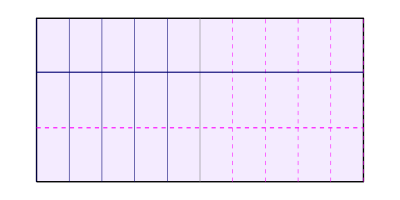

```mathematica
Module[{xmin,xmax,ymin,ymax,p1,p2,p3,p4,dr},
{xmin,xmax,ymin,ymax}={0,2,0,1};
p1={xmin,ymin};
p2={xmax,ymin};
p3={xmax,ymax};
p4={xmin,ymax};
Graphics[{
Style[Polygon[{p1,p2,p3,p4}],PaperWhiteSideFill],
Style[Line[{p1,p2,p3,p4,p1}],BorderLine],
Table[Style[Line[{(1-t)p1+t p2,(1-t)p4+t p3}],Which[t>1/2,ValleyRulingLine,t<1/2,MountainRulingLine,True,CreaseLine]],{t,0,1,1/10}],
Style[Line[{.67 p1+.33p4,.67p2+.33p3}],ValleyLine],
Style[Line[{.33 p1+.67p4,.33p2+.67p3}],MountainLine],
{}}]/.OrigamiStyle[]
]
```

Example FF with rulings.

```mathematica
DynamicModule[{cc,du,dr},
Manipulate[
cc={Cos[r #1],#1+#2,Sin[r #1]}&;(* a helix *)
du=π/50;(* divisions for rendering smooth surface *)
dr=π/10;(* divisions for rending rulings *)
Graphics3D[{
InvisibleCube[{0,0,0},1],
Table[Style[Polygon[{cc[u-du,-1],cc[u,-1],cc[u,+1],cc[u-du,+1]}],Paper3DFill],{u,0+du,2π,du}],
Style[Line[Table[cc[u,-1],{u,0,2π,du}]],BorderLine],
Style[Line[Table[cc[u,+1],{u,0,2π,du}]],BorderLine],
Style[Line[{cc[0,-1],cc[0,+1]}],BorderLine],
Style[Line[{cc[2π,-1],cc[2π,+1]}],BorderLine],
Table[Style[Line[{cc[u,-1],cc[u,+1]}],UnfoldedLine],{u,0+dr,2π-dr,dr}],
{}},Lighting->"Neutral"]/.OrigamiStyle[]
,{{r,1},0,1}]
]//ShowExample
```

#### OrigamiSampleGraphics OrigamiSampleGraphics2D OrigamiSampleGraphics3D OrigamiSampleGraphicsTrio

OrigamiSampleGraphics returns a Graphics object that is a styled crease pattern.

```mathematica
OrigamiSampleGraphics=Graphics[{
Style[Polygon[{{0,0},{6,0},{6,2},{0,2}}],PaperWhiteSideFill],
Style[Line[{{0,0},{6,0},{6,2},{0,2},{0,0}}],BorderLine],
Style[Line[{{1,0},{3,2}}],ValleyLine],
Style[Line[{{2,0},{4,2}}],MountainLine],
Style[Line[{{4.5,2},{6,.5}}],ValleyLine],
Style[Line[{{5,0},{5,2}}],CreaseLine]
}];
```

```mathematica
OrigamiSampleGraphics/.OrigamiStyle[]//ShowExample
```

OrigamiSampleGraphics2D returns a Graphics object that is a styled folded form.

```mathematica
OrigamiSampleGraphics2D=Graphics[{
Style[Polygon[{{0,0},{1,0},{3,2},{0,2}}],PaperWhiteSideFill],
Style[Polygon[{{1,0},{3,2},{3,3},{1,1}}],PaperColoredSideFill],
Style[Polygon[{{1,1},{5,1},{5,1.5},{3.5,3},{3,3}}],PaperWhiteSideFill],
Style[Polygon[{{3.5,1.5},{5,1.5},{3.5,3}}],PaperColoredSideFill],
Style[Line[{{2,2},{0,2},{0,0},{1,0},{1,1},{5,1},{5,1.5},{3.5,1.5},{3.5,3},{3,3}}],BorderLine],
Style[Line[{{1,0},{2,1}}],FoldedLine],
Style[Line[{{2,1},{3,2}}],HiddenFoldedLine],
Style[Line[{{2,2},{3,2},{3,3}}],HiddenBorderLine],
Style[Line[{{1,1},{3,3}}],FoldedLine],
Style[Line[{{3.5,3},{5,1.5}}],FoldedLine],
Style[Line[{{4,1},{4,1.5}}],UnfoldedLine],
Style[Line[{{4,1.5},{4,2.5},{3.5,2.5}}],HiddenUnfoldedLine]
}];
```

```mathematica
OrigamiSampleGraphics2D/.OrigamiStyle[]//ShowExample
```

OrigamiSampleGraphics3D returns a Graphics3D object that is a styled folded form.

```mathematica
OrigamiSampleGraphics3D=Graphics3D[{
Style[Polygon[{{0,0,0},{1,0,0},{3,2,0},{0,2,0}}],Paper3DFill],
Style[Polygon[{{1,0,0},{1,2,1},{3,4,1},{3,2,0}}],Paper3DFill],
Style[Polygon[{{1,2,1},{5,2,1},{5,4,1},{3,4,1}}],Paper3DFill],
Style[Line[{{1,0,0},{3,2,0}}],FoldedLine],
Style[Line[{{1,2,1},{3,4,1}}],FoldedLine],
Style[Line[{{3,2,0},{0,2,0},{0,0,0},{1,0,0},{1,2,1},{5,2,1},{5,4,1},{3,4,1},{3,2,0}}],BorderLine],
Style[Line[{{4,2,1},{4,4,1}}],CreaseLine]
}];
```

```mathematica
OrigamiSampleGraphics3D/.OrigamiStyle[]//ShowExample
```

OrigamiSampleGraphicsTrio returns a GraphicsRow object that displays example of all of the origami style objects in 2D and 3D. Good for testing and calibrating color and/or style overrides with different style settings.

```mathematica
OrigamiSampleGraphicsTrio=GraphicsRow[{
OrigamiSampleGraphics,
OrigamiSampleGraphics2D,
OrigamiSampleGraphics3D}];
```

Example

```mathematica
(temp=OrigamiSampleGraphicsTrio/.OrigamiStyle[])//ShowExample
```

```mathematica
Export[ExamplesDir[]<>"OrigamiSampleGraphicsTrio.pdf",temp,ImageSize->768]//ShowExample
```

For some unexplained reason, the hidden lines are getting lost when we wrap these objects in GraphicsRow[]. So a better rendition is obtained using ShowOrigamiSamples, next.

Note: the bug only seems to be in the screen rendering. Exported images contain the dotted lines properly.

#### OrigamiSwatchGraphics

OrigamiSwatchGraphics is a Graphics object that is a simple swatch of fills and lines, useful for color-matching in other programs.

```mathematica
OrigamiSwatchGraphics=Graphics[{
Style[Polygon[{{0,0},{1,0},{1,1},{0,1}}],{EdgeForm[],PaperWhiteSideFill}],
Style[Polygon[{{1.5,0},{2.5,0},{2.5,1},{1.5,1}}],{EdgeForm[],PaperColoredSideFill}],
Style[Line[{{0,1.5},{1,1.5}}],ValleyLine],
Style[Line[{{1.5,1.5},{2,1.5},{2.5,1.5}}],MountainLine],
{}}];
```

Example

```mathematica
(temp=OrigamiSwatchGraphics/.OrigamiStyle[])//ShowExample
```

```mathematica
Export[ExamplesDir[]<>"OrigamiSwatchGraphics.pdf",temp,ImageSize->256]//ShowExample
```

#### ShowOrigamiSamples[stylerules]

```mathematica
ShowOrigamiSamples[stylerules_]:=Module[{},
Print[OrigamiSampleGraphics/.stylerules];
Print[OrigamiSampleGraphics2D/.stylerules];
Print[OrigamiSampleGraphics3D/.stylerules]
]
```

Examples. Default rules.

```mathematica
ShowOrigamiSamples[OrigamiStyle[]]//ShowExample
```

Default styling shows everything, but is unrealistic in 2D because with transparency, the two-color paper does somewhat weird things.

Normally you’ll use either (two-color paper+opaque) or (single-color paper+transparency).

To display true two-color images, set WhiteSideColor and ColoreSideColor to two different values and set both opacities to 1, and turn off hidden line display.

```mathematica
ShowOrigamiSamples[OrigamiStyle[
WhiteSideColor->RGBColor[0.8,0.8,1],
ColoredSideColor->RGBColor[.3,.3,1],
Opacity2D->1,
Opacity3D->1,
ShowHidden->False
]]//ShowExample
```

To display overlapping layers in tessellations, set both sides to the same lightish color and turn down the opacity. You’ll probably want to leave hidden lines displaying to add emphasis to the transparent/overlapping layers.

```mathematica
ShowOrigamiSamples[OrigamiStyle[
WhiteSideColor->RGBColor[.6,1,.6],
ColoredSideColor->RGBColor[.6,1,.6],
Opacity2D->.25,
Opacity3D->.85
]]//ShowExample
```

#### ScoringStyle[opts] (options) MountainColor, ValleyColor, BorderColor, ScoreLineThickness

ScoringStyle[opts] returns a list of styles that assigns colors for laser-scored patterns: blue for mountain, red for valley, black for the border, and all hairline thickness. Any remaining CreaseLine, HiddenBorderLine, HiddenFoldedLine, HiddenUnfoldedLine, UnfoldedLine, or NoLine lines are wiped out because they shouldn't be scored (although the Hidden* lines are not used in crease patterns anyhow). Options are:
	MountainColor → color, specifies the color of mountain fold lines.
	ValleyColor → color, specifies the color of mountain fold lines.
	BorderColor → color, specifies the color of mountain fold lines.
	ScoreLineThickness → th, specifies the absolute thickness in points of all lines.

```mathematica
ScoreLineThickness::usage="ScoreLineThickness is an option to ScoringStyle that sets the thickness, in points, of scoring lines.";
```

```mathematica
Options[ScoringStyle]={
MountainColor->Blue,
ValleyColor->Red,
BorderColor->Black,
ScoreLineThickness->1
};
```

```mathematica
ScoringStyle[opts___]:=Module[{mc,vc,bc,st,x},
mc=MountainColor/.{opts}/.Options[ScoringStyle];
vc=ValleyColor/.{opts}/.Options[ScoringStyle];
bc=BorderColor/.{opts}/.Options[ScoringStyle];
st=ScoreLineThickness/.{opts}/.Options[ScoringStyle];
{BorderLine->{bc,AbsoluteThickness[st]},
ValleyLine->{vc,AbsoluteThickness[st]},
MountainLine->{mc,AbsoluteThickness[st]},
Style[___,CreaseLine,___]->Sequence[],
Style[___,FoldedLine,___]->Sequence[],
ValleyRulingLine->{vc,AbsoluteThickness[st]},
MountainRulingLine->{mc,AbsoluteThickness[st]},
Style[___,UnfoldedLine,___]->Sequence[],
Style[___,NoLine,___]->Sequence[],
Style[___,HiddenBorderLine,___]->Sequence[],
Style[___,HiddenFoldedLine,___]->Sequence[],
Style[___,HiddenUnfoldedLine,___]->Sequence[],
Style[___,PaperWhiteSideFill,___]->Sequence[],
Style[___,PaperColoredSideFill,___]->Sequence[],
Style[___,Paper3DFill,___]->Sequence[],
Style[___,Paper3DFillReversed,___]->Sequence[],
Style[___,Paper3DFillBothWhite,___]->Sequence[],
Style[___,Paper3DFillBothColored,___]->Sequence[]
}]
```

Example. Compare OrigamiStyle with ScoringStyle[].

```mathematica
Module[{test},
test=Graphics[{
Style[Line[{{0,.25},{1,.25}}],MountainLine],
Style[Line[{{0,.5},{1,.5}}],CreaseLine],
Style[Line[{{0,.75},{1,.75}}],ValleyLine],
Style[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],BorderLine]
}];
GraphicsRow[{
test/.OrigamiStyle[],
 test/.ScoringStyle[], 
test/.ScoringStyle[ScoreLineThickness->0.216]}]
]//ShowExample
```

#### OripaStyle[opts] (options) MountainColor, ValleyColor, CreaseColor, BorderColor, FoldedColor, WhiteSideColor, ColoredSideColor

OripaStyle[opts] returns a list of styles that assigns colors the way Oripa does: red for mountain, blue for valley, gray for unfolded creases, black for the border.

```mathematica
Options[OripaStyle]={
MountainColor->Red,
ValleyColor->Blue,
CreaseColor->Gray,
BorderColor->Black,
FoldedColor->Darker[Gray],
WhiteSideColor->GrayLevel[0.9],
ColoredSideColor->GrayLevel[0.7]
};
```

```mathematica
OripaStyle[opts___]:=Module[{mc,vc,cc,bc,fc,wsc,csc,x},
mc=MountainColor/.{opts}/.Options[OripaStyle];
vc=ValleyColor/.{opts}/.Options[OripaStyle];
cc=CreaseColor/.{opts}/.Options[OripaStyle];
bc=BorderColor/.{opts}/.Options[OripaStyle];
fc=FoldedColor/.{opts}/.Options[OripaStyle];
wsc=WhiteSideColor/.{opts}/.Options[OripaStyle];
csc=ColoredSideColor/.{opts}/.Options[OripaStyle];
{BorderLine->{bc,AbsoluteThickness[1],CapForm["Round"],JoinForm["Round"]},
ValleyLine->{vc,AbsoluteThickness[1],CapForm["Round"],JoinForm["Round"]},
MountainLine->{mc,AbsoluteThickness[1],CapForm["Round"],JoinForm["Round"]},
CreaseLine->{cc,AbsoluteThickness[.5],CapForm["Round"],JoinForm["Round"]},
FoldedLine->{fc,AbsoluteThickness[1],CapForm["Round"],JoinForm["Round"]},
UnfoldedLine->{cc,AbsoluteThickness[.5],CapForm["Round"],JoinForm["Round"]},
HiddenBorderLine->{bc,AbsoluteThickness[1],CapForm["Round"],JoinForm["Round"]},
HiddenFoldedLine->{fc,AbsoluteThickness[1],CapForm["Round"],JoinForm["Round"]},
HiddenUnfoldedLine->{cc,AbsoluteThickness[.5],CapForm["Round"],JoinForm["Round"]},
ValleyRulingLine->{vc,AbsoluteThickness[.5],CapForm["Round"],JoinForm["Round"]},
MountainRulingLine->{mc,AbsoluteThickness[.5],CapForm["Round"],JoinForm["Round"]},
PaperWhiteSideFill->{EdgeForm[],FaceForm[wsc]},
PaperColoredSideFill->{EdgeForm[],FaceForm[csc]},
Paper3DFill->{EdgeForm[],FaceForm[wsc,csc]},
Paper3DFillReversed->{EdgeForm[],FaceForm[csc,wsc]},
Paper3DFillBothWhite->{EdgeForm[],FaceForm[wsc,wsc]},
Paper3DFillBothColored->{EdgeForm[],FaceForm[csc,csc]}
}]
```

Example. Compare OrigamiStyle with ScoringStyle and OripaStyle.

```mathematica
Module[{test},
test=Graphics[{
Style[Polygon[{{0,0},{1,0},{1,1},{0,1},{0,0}}],Paper3DFill],
Style[Line[{{0,.25},{1,.25}}],MountainLine],
Style[Line[{{0,.5},{1,.5}}],CreaseLine],
Style[Line[{{0,.75},{1,.75}}],ValleyLine],
Style[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],BorderLine]
}];
GraphicsRow[{
test/.OrigamiStyle[], 
test/.ScoringStyle[],
 test/.OripaStyle[]}]
]//ShowExample
```

### Lighting utilities

#### Notes

With paper having a light side and a colored side, we want the true colors to show, so we want to use neutral lighting. Often, though, Mathematica’s default Lighting→”Neutral” washes out any shading on the white side of the paper. To deal with this, we provide the NeutralLighting function that can be used to turn down the lighting to an acceptable level.

#### NeutralLighting[r]

NeutralLighting[r] dims the default “Neutral” lighting by a factor r.

```mathematica
NeutralLighting[r_]:={
{"Ambient",RGBColor[0.35r,0.35r,0.35r]},{"Directional",RGBColor[0.37r,0.37r,0.37r],ImageScaled[{2,0,2}]},{"Directional",RGBColor[0.37r,0.37r,0.37r],ImageScaled[{2,2,2}]},{"Directional",RGBColor[0.37r,0.37r,0.37r],ImageScaled[{0,2,2}]}}
```

Example

```mathematica
Module[{g},
g=OrigamiSampleGraphics3D;
GraphicsRow[{
Show[g],
Show[g,Lighting->NeutralLighting[.75]],
Show[g,Lighting->NeutralLighting[.5]]}]/.OrigamiStyle[]
]//ShowExample
```

### 2D or 3D styled Graphics/Graphics3D elements

#### StyledPoint[p, opts] (options) PointStyle

StyledPoint[p, opts] creates a Point[p] wrapped in the given style directive.

```mathematica
PointStyle::usage="PointStyle is an option to StyledPoint that specifies style directives for the point.";
```

```mathematica
Options[StyledPoint]={
PointStyle->{}
};
```

```mathematica
StyledPoint[p_,opts___]:=Module[{ps},
ps=PointStyle/.{opts}/.Options[StyledPoint];
Style[Point[p],ps]
]
```

Example

```mathematica
Graphics[{
StyledPoint[{0,0}]
}]/.OrigamiStyle[]//ShowExample
```

#### StyledLine[rlist, opts] (options) LineStyle

StyledLine[rlist, opts] takes a list of points rlist and produces a styled line with the given Style directive. Options are:
	LineStyle→style, specifies the styling in the Style directive to use for the line.

```mathematica
Options[StyledLine]={
LineStyle->{}
};
```

```mathematica
StyledLine[rlist_,opts___]:=Module[{ls},
ls=LineStyle/.{opts}/.Options[StyledLine];
Style[Line[rlist],ls]
]
```

Example

```mathematica
Graphics[{
StyledLine[{{0,0},{1,0}},LineStyle->MountainLine],
StyledLine[{{0,1},{1,1}},LineStyle->ValleyLine],
StyledLine[{{0,0},{1,1}}]
}]/.OrigamiStyle[]//ShowExample
```

#### StyledVector[{p1, p2}, opts] StyledVector[p, d, opts] (options) VectorThickness, VectorArrowheads, VectorColor, VectorLabel

StyledVector[{p1, p2}, opts] produces a list of Graphics or Graphics3D primitives that render an arrow that represents a vector from p1 to p2 with an optional label at the arrow tip.

Options:
 	VectorThickness → th, specifies the thickness of the vector.
	VectorArrowheads → size, specifies the size of the arrowhead relative to the thickness.
	VectorColor → color, specifies the color of the vector.
	VectorLabel → {x, y, z}, labels to put at the end of the vector.

Returns a list of Graphics or Graphics3D elements, depending on the dimensionality of p1 and p2.

```mathematica
VectorThickness::usage="VectorThickness is an option to StyledVector that specifies the thickness of the vector.";
```

```mathematica
VectorArrowheads::usage="VectorArrowheads is an option to StyledVector that specifies the size of the arrowhead relative to the width of the graphic.";
```

```mathematica
VectorColor::usage="VectorColor is an option to StyledVector that specifies the color of the vector.";
```

```mathematica
VectorLabel::usage="VectorLabel is an option to StyledVector that specifies the label at the tip of the vector.";
```

```mathematica
Options[StyledVector]={
VectorThickness->.02,
VectorArrowheads->.04,
VectorColor->Black,
VectorLabel->""
};
```

```mathematica
StyledVector::badpts="The point pair `1` is not a pair of 2- or 3-vectors.";
```

```mathematica
StyledVector[{p1_List,p2_List},opts___]:=Module[{vt,vc,vl,vh},
vt=VectorThickness/.{opts}/.Options[StyledVector];
vc=VectorColor/.{opts}/.Options[StyledVector];
vl=VectorLabel/.{opts}/.Options[StyledVector];
vh=VectorArrowheads/.{opts}/.Options[StyledVector];
{Which[
Length[p1]==2&&Length[p2]==2,
Style[Arrow[{p1,p2}],{Thickness[vt],Arrowheads[vh], vc}],
Length[p1]==3&&Length[p2]==3,
Style[Arrow[Tube[{p1,p2},vt/2]],{Arrowheads[vh], vc}],
True,Message[StyledVector::badpts,{p1,p2}];Abort[]],
If[vl≠"",Text[vl,p2,{-2,0}],{}]}]
```

StyledVector[p, d, opts] does the same with the vector starting at p and extending in direction d.

```mathematica
StyledVector[p_List,d_List,opts___]:=StyledVector[{p,p+d},opts]
```

2D example.

```mathematica
Module[{p1,p2},
p1={0,0};
p2={1,1};
Graphics[StyledVector[{p1,p2},VectorLabel->"p"],Frame->True]
]//ShowExample
```

3D example.

```mathematica
Module[{p,d},
p={0,0,0};
d={1,1,1};
Graphics3D[StyledVector[p,d,VectorLabel->"q"],Boxed->True]
]//ShowExample
```

### 2D styled Graphics elements

#### Styled2DArc[r_1,r_2,opts] (options) ArcLabel, ArcLabelRadius, LineStyle

Styled2DArc[r_1,r_2,opts] returns a list of Graphics primitives that give a 2D "pie slice" extending counterclockwise from direction r_1 to r_2. Options are:
	ArcLabel→label, specifies that the middle of the arc is to be labeled with the graphics primitive label.
	ArcLabelRadius→r, specifies that the label is placed a distance r from the center of the unit circle.

```mathematica
ArcLabel::usage="ArcLabel is an option to Styled2DArc that specifies a label to be placed in the middle of the arc.";
```

```mathematica
ArcLabelRadius::usage="ArcLabelRadius is an option to Styled2DArc that specifies the distance from the center that the label should be placed.";
```

```mathematica
LineStyle::usage="LineStyle is an option to Styled2DArc that specifies the styling to apply to the arc line. It should be one of the predefined origami line styles.";
```

```mathematica
Options[Styled2DArc]={
ArcLabel->None,
ArcLabelRadius->0.2,
LineStyle->{}
};
```

```mathematica
Styled2DArc[r1_List,r2_List,opts___]:=Module[{α,alr,as,q1,q2,dq},
α=ArcLabel/.{opts}/.Options[Styled2DArc];
alr=ArcLabelRadius/.{opts}/.Options[Styled2DArc];
as=LineStyle/.{opts}/.Options[Styled2DArc];
q1=ArcTan@@r1;
q2=ArcTan@@r2;
dq=Mod[q2-q1,2π];
{Style[Circle[{0,0},1,{q1,q1+dq}],as],
If[α===None,{},Text[α,alr U[q1+dq/2]]]
}]
```

Example

```mathematica
Graphics[Styled2DArc[{1,0},{-1,-1},ArcLabel->"A"],
PlotRange->{{-1,1},{-1,1}},Axes->True]/.OrigamiStyle[]//ShowExample
```

Example with an origami style line.

```mathematica
Graphics[Styled2DArc[{1,0},{-1,-1},ArcLabel->Style["A",24, Red],LineStyle->ValleyLine],
PlotRange->{{-1,1},{-1,1}},Axes->True]/.OrigamiStyle[]//ShowExample
```

#### Styled2DAxes[opts] Styled2DAxes[xmax, ymax, zmax, opts] Styled2DAxes[{xmin, xmax}, {ymin, ymax}, {zmin, zmax}, opts] (options) AxesThickness, AxesArrowheads, AxesColor, AxesLabel

Styled2DAxes[{xmin, xmax}, {ymin, ymax}, opts] produces a list of Graphics primitives that render 2D axes. Options are:
	AxesThickness → th, specifies the thickness of the axes.
	AxesArrowheads → size, specifies the size of the arrowhead relative to the width of the graphic.
	AxesColor → color, specifies the color of the axes.
	AxesLabel → {x, y}, labels to put at the end of the positive-pointing axes (same option as in Graphics)
It returns a list of Graphics elements.

Styled2DAxes[xmax, ymax, opts] produces a list of Graphics primitives that render 2D axes, emanating from the origin.

Styled2DAxes[opts] produces a list of Graphics primitives that render 2D axes, emanating from the origin of unit length.

Use this when we want a more schematic form of axes without the tics from the default Mathematica axes.

```mathematica
AxesThickness::usage="AxesThickness is an option to Styled2DAxes that specifies the thickness of the axes and arrowheads.";
```

```mathematica
AxesArrowheads::usage="AxesArrowheads is an option to Styled2DAxes that specifies the size of the arrowhead relative to the thickness of the line.";
```

```mathematica
AxesColor::usage="AxesColor is an option toStyled2DAxes that specifies the color of the axes and arrowheads.";
```

```mathematica
Options[Styled2DAxes]={
AxesThickness->0.015,
AxesArrowheads->0.04,
AxesColor->Gray,
AxesLabel->{"x","y"}
};
```

```mathematica
Styled2DAxes[opts___]:=Styled2DAxes[1,1,opts]
```

```mathematica
Styled2DAxes[xmax_, ymax_, opts___]:=Styled2DAxes[{0, xmax}, {0, ymax},  opts]/;NumericQ[xmax]&&NumericQ[ymax]
```

```mathematica
Styled2DAxes[{xmin_, xmax_}, {ymin_, ymax_},  opts___]:=Module[{al,at,ac,ah},
at=AxesThickness/.{opts}/.Options[Styled2DAxes];
ah=AxesArrowheads/.{opts}/.Options[Styled2DAxes];
ac=AxesColor/.{opts}/.Options[Styled2DAxes];
al=AxesLabel/.{opts}/.Options[Styled2DAxes];
{StyledVector[{{xmin,0},{xmax,0}},VectorThickness->at,VectorArrowheads->ah,VectorColor->ac,VectorLabel->al⟦1⟧],
StyledVector[{{0,ymin},{0,ymax}},VectorThickness->at,VectorArrowheads->ah,VectorColor->ac,VectorLabel->al⟦2⟧]}]
```

Example

```mathematica
Module[{},
Graphics[Styled2DAxes[]]
]//ShowExample
```

```mathematica
Module[{},
Graphics[{
Styled2DAxes[1.3,1],
Style[Point[{0,0}],Red],
Style[Point[{1.3,0}],Green],
Style[Point[{0,1}],Blue],
{}}]
]//ShowExample
```

### 3D styled Graphics3D elements

#### Styled3DArc[r1, r2, opts] (options) ArcLabel, LineStyle, FillStyle, ArcDivisions, ArcMaximumAngle, ArcMethod, ArcDirection, RotationAxis

Styled3DArc[r1, r2, opts] returns a list of Graphics3D primitives that give a 3D "pie slice" extending from one direction vector to another.

Arguments:
	r1 — the source point.
	r2 — the destination point.

Options:
	ArcLabel → label specifies that the middle of the arc should be labeled with the graphics primitive label.
	LineStyle → style | None, specifies the style to use for the arc line.
	FillStyle → style | None, specifies the style to use for the polygonal wedge.
	Options[PolygonalEllipseArc3D] are passed through.

Returns a list of styled Graphics3D elements that represent the desired arc.

The length of the slice tapers linearly with angle. For simplicity of implementation, we assume that the angle is always less than π (which will be the case in degree-4 vertices).

See also PolygonalEllipseArc2D and PolygonalEllipseArc3D.

```mathematica
FillStyle::usage="FillStyle is an option to many styled graphics functions that specifies the fill style to use for polygons.";
```

```mathematica
Options[Styled3DArc]={
ArcLabel->None,
LineStyle->{},
FillStyle->None
};
```

```mathematica
Styled3DArc[r1_List, r2_List,opts___]:=Module[{al,ls,fs,m1,m2,x,y,z,a,arc},
al=ArcLabel/.{opts}/.Options[Styled3DArc];
ls=LineStyle/.{opts}/.Options[Styled3DArc];
fs=FillStyle/.{opts}/.Options[Styled3DArc];
m1=Mag[r1];
m2=Mag[r2];
x=r1/m1;
y=NormalizeReal[r2-(x.r2)x];
z=x~Cross~y;
a=ArcTan[x.r2,y.r2];
arc=PolygonalEllipseArc3D[r1,r2,opts];
{If[fs===None,{},Style[Polygon[{{0,0,0}}~Join~arc~Join~{{0,0,0}}],fs]],
If[ls===None,{},Style[Line[arc],ls]],
If[al===None,{},Text[al,m1^(1/2)m2^(1/2)U[0.5 a].{x,y}]]}]
```

Examples

```mathematica
Graphics3D[Styled3DArc[{1,0,0},{0,1,0},ArcLabel->Style["A",Italic,FontSize->16],FillStyle->Gray]]//ShowExample
```

```mathematica
Graphics3D[Styled3DArc[{1,0,0},{0,1,0},ArcLabel->Style["A",Italic,FontSize->16],FillStyle->Paper3DFillBothColored,LineStyle->MountainLine,FillStyle->Paper3DFill]]/.OrigamiStyle[]//ShowExample
```

```mathematica
Graphics3D[{
Styled3DArc[{1,0,0},{0,1,0},ArcLabel->"O",LineStyle->MountainLine,FillStyle->Paper3DFill],
Styled3DArc[{0,1,0},{0,0,1},ArcLabel->"R2D",LineStyle->ValleyLine,FillStyle->Paper3DFill],
Styled3DArc[{0,0,1},{1,0,0},ArcLabel->"T",LineStyle->CreaseLine,FillStyle->Paper3DFill]
},Boxed->False]/.OrigamiStyle[]//ShowExample
```

#### Styled3DArc[rlist, opts] (options) ArcLabel, LineStyle, FillStyle, ArcDivisions, ArcMaximumAngle, ArcMethod, ArcDirection, RotationAxis

Styled3DArc[rlist, opts] returns graphics primitives for a set of connected pie slices.

Options:
	Options[Styled3DArc] are passed through.

```mathematica
Styled3DArc[rlist_List,opts___]:=
Drop[MapThread[Styled3DArc[#1,#2,opts]&,{rlist,RotateLeft[rlist]},1],-1]
```

Example

```mathematica
Graphics3D[Styled3DArc[{{1,0,0},{0,1,0},{0,0,1}},FillStyle->Paper3DFill]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DArcClosed[rlist, opts] (options) ArcLabel, LineStyle, FillStyle, ArcDivisions, ArcMaximumAngle, ArcMethod, ArcDirection, RotationAxis

Styled3DArcClosed[rlist, opts] returns graphics primitives for a set of connected pie slices that closes a loop; thus, it can be used for a spherical vertex or for a trace on the Gaussian sphere.

Options:
	Options[Styled3DArc] are passed through.

```mathematica
Styled3DArcClosed[rlist_List,opts___]:=
MapThread[Styled3DArc[#1,#2,opts]&,{rlist,RotateLeft[rlist]},1]
```

Example

```mathematica
Graphics3D[Styled3DArcClosed[{{1,0,0},{0,1,0},{0,0,1}},FillStyle->Paper3DFill]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DDiskFromInPlaneVectors[p, {r1, r2}, r, opts] (options) ArcDivisions, LineStyle, FillStyle

Styled3DDiskFromInPlaneVectors[p, {r1, r2}, r, opts] returns the graphics primitives for a disk (a filled circle) based on its position, orientation, and radius.

Arguments:
	p — the center of the disk.
	{r1, r2} — direction vectors that define the plane of the disk. They don’t have to be normalized or orthogonal.
	r — the radius of the disk,

Options are:
	ArcDivisions→n, specifies the number of points to use in drawing the circle.
	LineStyle→style | None, specifies the Style directive to use in outlining the disk or None for no outline.
	FillStyle→style | None, specifies the Style directive to use in drawing the disk or None for no fill.

Returns a list of Graphics3D elements that represent the disk.

```mathematica
Options[Styled3DDiskFromInPlaneVectors]={
ArcDivisions->200,
LineStyle->{},
FillStyle->{}
};
```

```mathematica
Styled3DDiskFromInPlaneVectors[p_List,{r1_List,r2_List},r_,opts___]:=Module[{ad,ls,fs,x,y,z,pts},
ad=ArcDivisions/.{opts}/.Options[Styled3DDiskFromInPlaneVectors];
ls=LineStyle/.{opts}/.Options[Styled3DDiskFromInPlaneVectors];
fs=FillStyle/.{opts}/.Options[Styled3DDiskFromInPlaneVectors];
x=NormalizeReal[r1];
z=NormalizeReal[r1×r2];
y=z×x;
pts=p+r#&/@ Table[x Cos[ϕ] + y Sin[ϕ],{ϕ,0,2π,2π/ad}];
{If[fs===None,{},Style[Polygon[pts],fs]],If[ls===None,{},Style[Line[pts],ls]]}
]
```

Examples

```mathematica
Graphics3D[Styled3DDiskFromInPlaneVectors[{0,0,0},{{1,0,0},{1,1,0}},1]]//ShowExample
```

```mathematica
Graphics3D[Styled3DDiskFromInPlaneVectors[{0,0,0},{{1,0,0},{1,1,0}},1,LineStyle->BorderLine,FillStyle->Paper3DFill]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DDisk[p, n, r, opts] (options) ArcDivisions, LineStyle, FillStyle

Styled3DDisk[p, n, r, opts] constructs a styled circular disk from its center, normal vector, and radius.

Arguments:
	p — the center of the disk.
	n — the normal vector of the disk.
	r — the radius of the disk.

Options:
	ArcDivisions → n, specifies the number of points to use in drawing the circle.
	LineStyle→style | None, specifies the Style directive to use in outlining the disk or None for no outline.
	FillStyle→style | None, specifies the Style directive to use in drawing the disk or None for no fill.

Returns Graphics3D elements that represent the disk.

```mathematica
Styled3DDisk[p_List,n_List,r_,opts___]:=Module[{nx, ny,n1,n2},
nx=n×{1,0,0};
ny=n×{0,1,0};
If[Mag[nx]>Mag[ny],n1=NormalizeReal[nx],n1=NormalizeReal[ny]];
n2=n×n1;
Styled3DDiskFromInPlaneVectors[p,{n1,n2},r,opts]
]
```

Example

```mathematica
Graphics3D[Styled3DDisk[{0,0,0},{1,1,0},1]]//ShowExample
```

```mathematica
Graphics3D[Styled3DDisk[{0,0,0},{1,1,0},1,LineStyle->CreaseLine,FillStyle->Paper3DFill]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DUnitCircleFromInPlaneVectors[r1, r2, opts] [deprecated] (options) ArcDivisions, LineStyle

Styled3DUnitCircleFromInPlaneVectors[r1, r2, opts] returns the graphics primitives for a unit circle in the plane defined by two vectors.

Arguments:
	r1, r2 — direction vectors that define the plane of the disk. They don’t have to be normalized or orthogonal.

Options:
	ArcDivisions → n, specifies the number of points to use in drawing the circle.
	LineStyle → style, specifies the Style directive for the line.

Returns Graphics3D elements that represent the disk.

```mathematica
Styled3DUnitCircleFromInPlaneVectors[r1_List,r2_List,opts___]:=Styled3DDiskFromInPlaneVectors[{0,0,0},{r1,r2},1,FillStyle->None,opts]
```

Examples.

```mathematica
Graphics3D[Styled3DUnitCircleFromInPlaneVectors[{1,0,0},{1,1,0}]]//ShowExample
```

```mathematica
Graphics3D[Styled3DUnitCircleFromInPlaneVectors[{1,0,0},{1,1,0},LineStyle->CreaseLine]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DUnitCircleFromNormal[n, opts] [deprecated] (options) ArcDivisions, LineStyle

Styled3DUnitCircleFromNormal[n, opts] returns the graphics primitives for a unit circle that is perpendicular to a direction vector.

Arguments:
	n — the normal vector of the disk.

Options:
	ArcDivisions → n, specifies the number of points to use in drawing the circle.
	LineStyle → style, specifies the Style directive for the line.

Returns Graphics3D elements that represent the disk.

```mathematica
Styled3DUnitCircleFromNormal[n_List,opts___]:=Styled3DDisk[{0,0,0},n,1,FillStyle->None,opts]
```

Example

```mathematica
Graphics3D[Styled3DUnitCircleFromNormal[{1,1,0}]]//ShowExample
```

```mathematica
Graphics3D[Styled3DUnitCircleFromNormal[{1,1,0},LineStyle->CreaseLine]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DUnitDiskFromInPlaneVectors[r1, r2, opts] [deprecated] (options) ArcDivisions, LineStyle, FillStyle

Styled3DUnitDiskFromInPlaneVectors[r1, r2, opts] returns the graphics primitives for a unit disk (i.e., a filled circle) in the plane spanned by two vectors.

Arguments:
	r1, r2 — direction vectors that define the plane of the disk. They don’t have to be normalized or orthogonal.

Options are:
	ArcDivisions → n, specifies the number of points to use in drawing the circle.
	LineStyle → style | None, specifies the Style directive to use in outlining the disk or None for no outline.
	FillStyle → style | None, specifies the Style directive to use in drawing the disk or None for no fill.

Returns Graphics3D elements that represent the disk.

```mathematica
Styled3DUnitDiskFromInPlaneVectors[r1_List,r2_List,opts___]:=Styled3DDiskFromInPlaneVectors[{0,0,0},{r1,r2},1,opts]
```

Examples

```mathematica
Graphics3D[Styled3DUnitDiskFromInPlaneVectors[{1,0,0},{1,1,0}]]//ShowExample
```

```mathematica
Graphics3D[Styled3DUnitDiskFromInPlaneVectors[{1,0,0},{1,1,0},LineStyle->BorderLine,FillStyle->Paper3DFill]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DUnitDiskFromNormal[n, opts] [deprecated] (options) ArcDivisions, LineStyle, FillStyle

Styled3DUnitDiskFromNormal[r, opts] returns the graphics primitives for a unit circle that is perpendicular to a vector.

Arguments:
	n — the normal vector of the disk.

Options:
	ArcDivisions → n, specifies the number of points to use in drawing the circle.
	LineStyle → style | None, specifies the Style directive to use in outlining the disk or None for no outline.
	FillStyle → style | None, specifies the Style directive to use in drawing the disk or None for no fill.

Returns Graphics3D elements that represent the disk.

```mathematica
Styled3DUnitDiskFromNormal[n_,opts___]:=Styled3DDisk[{0,0,0},n,1,opts]
```

Example

```mathematica
Graphics3D[Styled3DUnitDiskFromNormal[{1,1,0}]]//ShowExample
```

```mathematica
Graphics3D[Styled3DUnitDiskFromNormal[{1,1,0},LineStyle->CreaseLine,FillStyle->Paper3DFill]]/.OrigamiStyle[]//ShowExample
```

#### Styled3DSolidArrow[r_1,r_2,opts] [deprecated] (options) ArrowheadFraction, ArrowheadRadius, ArrowLabel, FillStyle

Styled3DSolidArrow[r_1,r_2,opts] returns a list of Graphics3D primitives that give an arrow with a conical tip. Useful for drawing vectors in 3D. Options are:
	ArrowheadFraction→r, specifies the fraction of the length to devote to the conical arrowhead.
	ArrowheadRadius→r, specifies the radius of the base of the arrow relative to its length.
	ArrowRadius→r, specifies the radius of the stem of the arrow relative to its length.
	FillStyle→r, specifies the fill style for all surfaces.

This is deprecated because Mathematica now directly supports 3D solid arrows via the Arrow[Tube[...]] construction. See example.

```mathematica
ArrowheadFraction::usage="ArrowheadFraction is an option to Styled3DSolidArrow that specifies the fraction of the length that should be used for the arrowhead.";
```

```mathematica
ArrowheadRadius::usage="ArrowheadRadius is an option ot Styled3DSolidArrow that specifies the radius of the base of the arrowhead.";
```

```mathematica
ArrowRadius::usage="ArrowRadius is an option to Styled3DSolidArrow that specifies the radius of the body of the arrow.";
```

```mathematica
ArrowLabel::usage="ArrowLabel is an option to Styled3DSolidArrow that specifies an label to place at the arrow ti.";
```

```mathematica
Options[Styled3DSolidArrow]={
ArrowheadFraction->0.333,
ArrowheadRadius->0.333,
ArrowRadius->0.25,
ArrowLabel->None,
FillStyle->{}
};
```

```mathematica
Styled3DSolidArrow[r1_List,r2_List,opts___]:=Module[{rr=Mag[r2-r1],ahf,ahr,ar,α,fs,rx},
ahf=ArrowheadFraction/.{opts}/.Options[Styled3DSolidArrow];
ahr=ArrowheadRadius/.{opts}/.Options[Styled3DSolidArrow];
ar=ArrowRadius/.{opts}/.Options[Styled3DSolidArrow];
α=ArrowLabel/.{opts}/.Options[Styled3DSolidArrow];
fs=FillStyle/.{opts}/.Options[Styled3DSolidArrow];
rx=ahf r1 + (1-ahf) r2;
{Style[{Cylinder[{r1,rx},ar ahf rr],Cone[{rx,r2},ahr ahf rr]},fs],If[α===None,{},Text[α,r2]]}]
```

Example

```mathematica
Graphics3D[{Styled3DSolidArrow[{0,0,0},{1,0,0},ArrowLabel->"x"],Styled3DSolidArrow[{0,0,0},{0,1,0},ArrowLabel->"y"],Styled3DSolidArrow[{0,0,0},{0,0,1},ArrowLabel->"z"]}]//ShowExample
```

Example -- 3D solid arrow using built-in Mathematica primitives.

```mathematica
Module[{x,y,z,ahf,ar},
x={{0,0,0},{1,0,0}};
y={{0,0,0},{0,1,0}};
z={{0,0,0},{0,0,1}};
ahf=0.1;
ar=0.04;
Graphics3D[{
Style[Arrow[Tube[x,ar]],Arrowheads[ahf], Red],
Style[Arrow[Tube[y,ar]],Arrowheads[ahf], Green],
Style[Arrow[Tube[z,ar]],Arrowheads[ahf], Blue]
}]
]//ShowExample
```

#### Styled3DAxes[opts] Styled3DAxes[xmax, ymax, zmax, opts] Styled3DAxes[{xmin, xmax}, {ymin, ymax}, {zmin, zmax}, opts] (options) AxesThickness, AxesArrowheads, AxesColor, AxesLabel

Styled3DAxes[{xmin, xmax}, {ymin, ymax}, {zmin, zmax}, opts] produces a list of Graphics3D primitives that render 3D axes. Options are:
	AxesThickness → th, specifies the thickness of the axes.
	AxesArrowheads → size, specifies the size of the arrowhead relative to the width of the graphics.
	AxesColor → color, specifies the color of the axes.
	AxesLabel → {x, y, z}, labels to put at the end of the positive-pointing axes (same option as in Graphics3D)
It returns a list of Graphics3D elements.

Styled3DAxes[xmax, ymax, zmax, opts] produces a list of Graphics3D primitives that render 3D axes that start at the origin.

Styled3DAxes[opts] produces a list of Graphics3D primitives that render 3D axes that start at the origin and have unit length.

```mathematica
Options[Styled3DAxes]={
AxesThickness->0.015,
AxesArrowheads->0.04,
AxesColor->Gray,
AxesLabel->{"x","y","z"}
};
```

```mathematica
Styled3DAxes[opts___]:=Styled3DAxes[1,1,1,opts]
```

```mathematica
Styled3DAxes[xmax_, ymax_, zmax_, opts___]:=Styled3DAxes[{0, xmax}, {0, ymax}, {0, zmax}, opts]/;(NumericQ[xmax]&&NumericQ[ymax]&&NumericQ[zmax])
```

```mathematica
Styled3DAxes[{xmin_, xmax_}, {ymin_, ymax_}, {zmin_, zmax_}, opts___]:=Module[{al,at,ac,ah},
at=AxesThickness/.{opts}/.Options[Styled3DAxes];
ah=AxesArrowheads/.{opts}/.Options[Styled3DAxes];
ac=AxesColor/.{opts}/.Options[Styled3DAxes];
al=AxesLabel/.{opts}/.Options[Styled3DAxes];
{StyledVector[{{xmin,0,0},{xmax,0,0}},VectorThickness->at,VectorArrowheads->ah,VectorColor->ac,VectorLabel->al⟦1⟧],
StyledVector[{{0,ymin,0},{0,ymax,0}},VectorThickness->at,VectorArrowheads->ah,VectorColor->ac,VectorLabel->al⟦2⟧],
StyledVector[{{0,0,zmin},{0,0,zmax}},VectorThickness->at,VectorArrowheads->ah,VectorColor->ac,VectorLabel->al⟦3⟧]}]
```

Examples.

```mathematica
Module[{},
Graphics3D[{Styled3DAxes[]}]
]//ShowExample
```

```mathematica
Module[{},
Graphics3D[{Styled3DAxes[1.7,1.3,1.0]}]
]//ShowExample
```

### Symbolically styled origami lines

#### StyledMountainLine[rlist]

StyledMountainLine[rlist] returns a styled Line with Style options that turn it into a crease pattern mountain fold line.

```mathematica
StyledMountainLine[rlist_List]:=Style[Line[rlist],MountainLine]
```

Example

```mathematica
Graphics[StyledMountainLine[{{0,0},{1,0},{1,1}}]]/.OrigamiStyle[]//ShowExample
```

#### StyledValleyLine[rlist]

StyledValleyLine[rlist] returns a styled Line with Style options that turn it into a crease pattern valley fold line.

```mathematica
StyledValleyLine[rlist_List]:=Style[Line[rlist],ValleyLine]
```

Example

```mathematica
Graphics[StyledValleyLine[{{0,0},{1,0},{1,1}}]]/.OrigamiStyle[]//ShowExample
```

#### StyledCreaseLine[rlist]

StyledCreaseLine[rlist] returns a styled Line with Style options that turn it into a crease pattern crease (unfolded) fold line.

```mathematica
StyledCreaseLine[rlist_List]:=Style[Line[rlist],CreaseLine]
```

Example

```mathematica
Graphics[StyledCreaseLine[{{0,0},{1,0},{1,1}}]]/.OrigamiStyle[]//ShowExample
```

#### StyledFoldLine[rlist, γ, opts] (options) MinimumAngle

StyledFoldLine[rlist, γ, opts] returns a styled Line with Style options that represent the specified dihedral angle γ, i.e., a mountain, valley, or crease line, depending on the angle. Note that this works with both 2D and 3D lines. Options are:
	MinimumAngle→gmin, where gmin is the magnitude of the dihedral angle below which the line will be represented as a crease (unfolded) line.

```mathematica
MinimumAngle::usage="MinimumAngle is an option to StyledFoldLine that specifies the minimum angle at which to render a mountain or valley line (as opposed to an unfolded crease line).";
```

```mathematica
Options[StyledFoldLine]={
MinimumAngle->1°
};
```

```mathematica
StyledFoldLine[rlist_List,gg_,opts___]:=Module[{gmin},
gmin=MinimumAngle/.{opts}/.Options[StyledFoldLine];
Which[
gg>gmin,StyledValleyLine[rlist],
gg<-gmin,StyledMountainLine[rlist],
True,StyledCreaseLine[rlist]]
]
```

Example

```mathematica
Graphics[{
StyledFoldLine[{{0,0},{1,0}},-30°],(* mountain *)
StyledFoldLine[{{0,0},{1,1}},0°], (* unfolded *)
StyledFoldLine[{{0,0},{0,1}},30°] (* valley *)
}]/.OrigamiStyle[]//ShowExample
```

#### StyledGenericFoldLine[rlist, γ, opts] (options) MinimumAngle

StyledGenericFoldLine[rlist,γ,opts] is similar to StyledFoldLine, but simply returns a FoldedLine or empty list, depending on the angle. Note that this works with both 2D and 3D lines. Options are:
	MinimumAngle→gmin, where gmin is the magnitude of the dihedral angle below which the line will not be represented.

```mathematica
Options[StyledGenericFoldLine]={
MinimumAngle->1°
};
```

```mathematica
StyledGenericFoldLine[rlist_List,gg_,opts___]:=Module[{gmin},
gmin=MinimumAngle/.{opts}/.Options[StyledFoldLine];
If[gg>gmin||gg<-gmin,Style[Line[rlist],FoldedLine],{}]]
```

Example. Compare this to the previous example.

```mathematica
Graphics[{
StyledGenericFoldLine[{{0,0},{1,0}},-30°],(* mountain *)
StyledGenericFoldLine[{{0,0},{1,1}},0°], (* unfolded *)
StyledGenericFoldLine[{{0,0},{0,1}},30°] (* valley *)
}]/.OrigamiStyle[]//ShowExample
```

### Destruction by style

#### KillCreases[expr]

KillCreases[expr] completely removes all CreaseLine lines.

Useful for turning a display pattern into a scored pattern, where don’t want to score on unfolded crease lines. You can also accomplish the same effect by applying rule CreaseLine→NoLine.

```mathematica
KillCreases[expr_]:=expr/.Style[_,CreaseLine]->Sequence[];
```

Example, show before and after side-by-side.

```mathematica
Module[{g},
g=Graphics[{Style[Line[{{0,0},{1,0}}],ValleyLine],Style[Line[{{0,.5},{1,.5}}],CreaseLine],Style[Line[{{0,1},{1,1}}],MountainLine]}];
GraphicsRow[{g,KillCreases[g]}]/.OrigamiStyle[]
]//ShowExample
```

#### KillBorder[expr]

KillBorder[expr] completely removes all BorderLine and HiddenBorderLine lines.

Useful particularly to display shapes where you don’t want to suggest a sharp edge of the paper, e.g., circular polygons twists. You can also accomplish the same effect by applying rules {BorderLine → NoLine, HiddenBorderLine → NoLine}.

```mathematica
KillBorder[expr_]:=expr/.{Style[_,BorderLine]->Sequence[],Style[_,HiddenBorderLine]->Sequence[]}
```

#### KillHidden[expr]

KillHidden[expr] completely removes all HiddenLine and HiddenBorderLine lines.

Useful particularly to display shapes where you don’t want to suggest a sharp edge of the paper, e.g., circular polygons twists. You can also accomplish the same effect by applying rules {HiddenFoldedLine → NoLine, HiddenUnfoldedLine → NoLine, HiddenBorderLine → NoLine}.

```mathematica
KillHidden[expr_]:=expr/.{Style[_,HiddenFoldedLine]->Sequence[],Style[_,HiddenUnfoldedLine]->Sequence[],Style[_,HiddenBorderLine]->Sequence[]}
```

### Reversing line and fill styles

#### Notes

Sometimes we’d like to change mountains to valleys or white side to colored after an object is constructed. These functions let us do that in CPs and FFs.

Note, though, that the functions need to be applied while styles are still symbolic, i.e., before the application of OrigamiStyle rules.

#### ReverseLineStyle[obj]

ReverseLineStyle[obj] swaps mountain and valley line styles.

```mathematica
ReverseLineStyle[obj_]:=obj/.{
MountainLine->ValleyLine,
ValleyLine->MountainLine,
MountainRulingLine->ValleyRulingLine,
ValleyRulingLine->MountainRulingLine};
```

Example.

```mathematica
GraphicsRow[{
OrigamiSampleGraphics,
OrigamiSampleGraphics//ReverseLineStyle
}/.OrigamiStyle[]]//ShowExample
```

#### ReverseFillStyle[obj]

ReverseFillStyle[obj] swaps white and colored side fill styles.

```mathematica
ReverseFillStyle[obj_]:=obj/.{
Paper3DFill->Paper3DFillReversed,
PaperWhiteSideFill->PaperColoredSideFill,
PaperColoredSideFill->PaperWhiteSideFill,
Paper3DFillBothWhite->Paper3DFillBothColored,
Paper3DFillBothColored->Paper3DFillBothWhite};
```

Example.

```mathematica
GraphicsGrid[{
{OrigamiSampleGraphics2D,OrigamiSampleGraphics2D//ReverseFillStyle},
{OrigamiSampleGraphics3D,OrigamiSampleGraphics3D//ReverseFillStyle}
}/.OrigamiStyle[]]//ShowExample
```

### 2D and 3D styled curves and patches

#### Notes

These styled elements are used primarily in renderings of curved  surfaces and folds. They take pure functions that represent smooth curves and surfaces and render space curves and surfaces, respectively.

#### Shadow ShadowHeight ShadowColor

One of the things that helps visualize a 3D shape is if it casts a shadow on the plane below it. Many of these functions support the options
	Shadow → True | False, specifies whether to cast a shadow
	ShadowHeight → z, specifies the height of the shadow plane.
	ShadowColor → color, specifies the color of the shadow.

```mathematica
Shadow::usage="Shadow is an option to StyledCurve and StyledPatch that specifies whether to add a shadow below the curve or patch. Only for 3D.";
```

```mathematica
ShadowHeight::usage="ShadowHeight is an option to StyledCurve and StyledPatch that specifies the height of the shadow below the curve or patch. Only for 3D.";
```

```mathematica
ShadowColor::usage="ShadowColor is an option to StyledCurve and StyledPatch that specifies the color of the shadow below the curve or patch. Only for 3D.";
```

#### Shadowify[expr, opts] (options) ShadowHeight, ShadowColor

Shadowify[expr, opts] takes a Graphics3D object and creates a flattened shadow of it.

The shadow is given a fixed color, independent of the lighting.

Note that Line and Polygon objects have different lighting models; Line colors are independent of lighting, while Polygon colors are affected by lighting, opacity, edge. So we have to do different conversions on Lines and Polygons.

For best results, Line and Polygon objects should be immediately enclosed by Style wrappers. If you do this, then they’ll end up with the same shadow color. If, however, you bury everything within a larger Style directive, then Lines will cast a Black shadow, independent of the ShadowColor option.

```mathematica
Options[Shadowify]={
ShadowHeight->0,
ShadowColor->LightGray
};
```

```mathematica
Shadowify[g_,opts___]:=Module[{sz,sc,gs},
sz=ShadowHeight/.{opts}/.Options[Shadowify];
sc=ShadowColor/.{opts}/.Options[Shadowify];
gs=FunctionTransform[g,{1,1,0}#+{0,0,sz}&];
gs/.{
Style[expr_Line,sopts___]:>Style[expr,sopts,sc,EdgeForm[]],
Style[expr_Polygon,sopts___]:>Style[expr,sopts,Glow[sc],Black,Opacity[1],EdgeForm[]],
Style[expr_,sopts___]:>Style[expr,sopts,Glow[sc],Black,Opacity[1],EdgeForm[]]}]
```

Example. Combining Line and Polygon properly.

```mathematica
Module[{g},
g={
Style[Line[{{0,0,.7},{1,0,.7},{1,1,.7},{.1,.1,1}}],Red,Thickness[.02]],
Style[Polygon[{{.25,.25,.3},{.75,.25,.3},{.75,.75,.3},{.25,.75,.3}}],Green],
Style[Polygon[{{.2,.2,.5},{.5,.2,.5},{.5,.5,.5},{.2,.5,.5}}],Blue],
{}};
Graphics3D[{g,Shadowify[g]}]
]//ShowExample
```

Example with symbolic styles.

```mathematica
Module[{g},
g={
Style[Line[{{0,0,.7},{1,0,.7},{1,1,.7},{.1,.1,1}}],ValleyLine],
Style[Polygon[{{.25,.25,.3},{.75,.25,.3},{.75,.75,.3},{.25,.75,.3}}],PaperWhiteSideFill],
Style[Polygon[{{.2,.2,.5},{.5,.2,.5},{.5,.5,.5},{.2,.5,.5}}],PaperColoredSideFill],
{}};
Graphics3D[{g,Shadowify[g]},Lighting->NeutralLighting[.5],ViewPoint->{10,-8,5}]/.OrigamiStyle[]
]//ShowExample
```

#### StyledCurve[c, {tmin, tmax}, opts] (options) CurveDivisions, LineStyle, Shadow, ShadowHeight, ShadowColor

StyledCurve[c, {tmin, tmax}, opts] produces Graphics or Graphics3D elements for a styled line that represents a curved line specified by a parametric function.

Arguments:
	c — a pure function that gives the 2D or 3D trajectory of the line.
	{tmin, tmax} — start and end values of the parameter.

Options:
	CurveDivisions → nt, the number of segments to use in the discretization of the curve.
	LineStyle → style | None, a named symbolic style to use for the curve, or a list of style directives.
	Shadow → True | False, specifies whether to add a shadow.
	ShadowHeight, ShadowColor are passed through to Shadowify.

Returns a list of elements describing the object.

LineStyle → None will not generate any elements. This is used by subsequent patch-drawing routines to specify whether to draw edges on the patch.

```mathematica
CurveDivisions::usage="CurveDivisions is an option to StyledCurve and other functions that specifies the number of segments to use in drawing a curved line or surface.";
```

```mathematica
Options[StyledCurve]={
CurveDivisions->100,
Shadow->False,
LineStyle->{Thickness[.015],Black}
};
```

```mathematica
StyledCurve[c_Function, {tmin_,tmax_},opts___]:=Module[{sh,nt,ls,dim,g},
nt=CurveDivisions/.{opts}/.Options[StyledCurve];
sh=Shadow/.{opts}/.Options[StyledCurve];
ls=LineStyle/.{opts}/.Options[StyledCurve];
dim=Length[c[tmin]];
g=If[ls===None,{},Style[Line[Table[c[t],{t,tmin,tmax,(tmax-tmin)/nt}]],ls]];
{g,If[dim==3&&sh,Shadowify[g,opts],{}]}]
```

Example.

```mathematica
Module[{c,stc},
c={Cos[#],Sin[#],.1#}&;
stc=StyledCurve[c,{0,4π},Shadow->True];
Graphics3D[stc]
]//ShowExample
```

Finer divisions, use a ValleyLine, add a shadow.

```mathematica
Module[{c,spl},
c={Cos[#],Sin[#],.1#}&;
spl=StyledCurve[c,{0,4π},LineStyle->ValleyLine,CurveDivisions->100,Shadow->True];
Graphics3D[spl]/.OrigamiStyle[]
]//ShowExample
```

Note that you can also give style directives explicitly in a list.

```mathematica
Module[{c,spl},
c={Cos[#],Sin[#],.1#}&;
spl=StyledCurve[c,{0,2π},LineStyle->{Blue,Thickness[.02]},Shadow->True];
Graphics3D[spl]/.OrigamiStyle[]
]//ShowExample
```

#### StyledPatch[s, {umin, umax}, {vmin, vmax}, opts] (options) PatchDivisions, FillStyle, OutlineStyle, Shadow, ShadowHeight, ShadowColor

StyledPatch[s, {umin, umax}, {vmin, vmax}, opts] produces Graphics or Graphics3D elements for a styled patch that represents a curved surface specified by a parametric function.

Arguments:
	s — a pure function of two variables that gives the surface in 2D or 3D.
	{umin, umax} — bounds on the first parameter.
	{vmin, vmax} — bounds on the second parameter.

Options:
	PatchDivisions → {nu, nv}, the number of divisions to use in the two parameters.
	Shadow → True | False, specifies whether to draw a shadow (3D only)
	FillStyle → style | None, specifies a named style or a list of style directives to use for the patch surface.
	OutlineStyle → style, specifies the named style to use for outlining the patch.
	ShadowHeight, ShadowColor are passed through to Shadowify.

Returns: a list of Style objects containing the graphics elements.

If Shadow → True, a shadow is generated only for 3D objects. If s produces 2D points, no shadow will be generated.

If FillStyle → None, then the polygons of the patch are not generated at all. If FillStyle → NoFill, they are generated, but OrigamiStyle[] will not render them. Other style settings might.

OutlineStyle → style has several forms that style could take:
	None — don’t outline the patch.
	style — a single named style to use for the entire outline.
	{style} — a single named style to use for the entire outline.
	{{style1, ...}} — multiple style directives to apply to the entire outline.
	{style1, style2, style3, style4} — styles to apply individually to the 4 sides (CCW order in the (u,v) plane, beginning with the v=0 line).

```mathematica
PatchDivisions::usage="PatchDivisions is an option to StyledPatch that specifies the number of divisions to use in the two directions for constructing the patch.";
```

```mathematica
OutlineStyle::usage="OutlineStyle is an option to StyledPatch that specifies the style(s) to use for outlining the patch.";
```

```mathematica
Options[StyledPatch]={
PatchDivisions->{50,50},
Shadow->False,
FillStyle->Paper3DFill,
OutlineStyle->None
};
```

```mathematica
StyledPatch::badline="`1` is an invalid format for the OutlineStyle option.";
```

```mathematica
StyledPatch[s_Function,{umin_,umax_},{vmin_,vmax_},opts___]:=Module[{nu,nv,fs,ls,dim,sh,pts,spts,polys,lines},
{nu,nv}=PatchDivisions/.{opts}/.Options[StyledPatch];
fs=FillStyle/.{opts}/.Options[StyledPatch];
ls=OutlineStyle/.{opts}/.Options[StyledPatch];
sh=Shadow/.{opts}/.Options[StyledPatch];
pts=Table[s[u,v],{u,umin,umax,(umax-umin)/nu},{v,vmin,vmax,(vmax-vmin)/nv}];
polys=If[fs===None,
{},
Table[{
(* triangulate quads because they could be skew quads and that confuses rendering *)
Style[Polygon[{pts⟦iu,iv⟧,pts⟦iu+1,iv⟧,pts⟦iu+1,iv+1⟧}],fs],Style[Polygon[{pts⟦iu+1,iv+1⟧,pts⟦iu,iv+1⟧,pts⟦iu,iv⟧}],fs]},{iu,nu},{iv,nv}]];
ls=Switch[Length[ls],
0,{ls,ls,ls,ls},
1,If[Head[ls⟦1⟧]===List,{ls⟦1,1⟧,ls⟦1,1⟧,ls⟦1,1⟧,ls⟦1,1⟧},{ls⟦1⟧,ls⟦1⟧,ls⟦1⟧,ls⟦1⟧}],
4,ls,
_,Message[StyledPatch::badline,ls];Abort[]];
dim=Length[s[umin,vmin]];
{polys,
If[dim==3&&sh,Shadowify[polys,opts],{}],
If[ls⟦1⟧===None,{},Style[Line[Table[pts⟦iu,1⟧,{iu,nu+1}]],ls⟦1⟧]],
If[ls⟦2⟧===None,{},Style[Line[Table[pts⟦nu+1,iv⟧,{iv,nv+1}]],ls⟦2⟧]],
If[ls⟦3⟧===None,{},Style[Line[Table[pts⟦iu,nv+1⟧,{iu,nu+1}]],ls⟦3⟧]],
If[ls⟦4⟧===None,{},Style[Line[Table[pts⟦1,iv⟧,{iv,nv+1}]],ls⟦4⟧]],
{}}]
```

Example, 2D.

```mathematica
Module[{s,spp},
s={#1,#2}&;
spp=StyledPatch[s,{-1,1},{-1,1}];
Graphics[spp]/.OrigamiStyle[]
]//ShowExample
```

Example, 3D.

```mathematica
Module[{s,spp},
s={#1,#2,.5(1-(#1^2+#2^2))}&;
spp=StyledPatch[s,{-1,1},{-1,1}];
Graphics3D[spp,Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

Example. Add outlining, coarser divisions, and a shadow.

```mathematica
Module[{s,spp},
s={#1,#2,.5(1-(#1^2+#2^2))}&;
spp=StyledPatch[s,{-1,1},{-1,1},OutlineStyle->FoldedLine,PatchDivisions->{5,5},Shadow->True,ShadowHeight->-.6];
Graphics3D[spp,Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

Different outlining on the four sides.

```mathematica
Module[{s,spp},
s={#1,#2,.5(1-(#1^2+#2^2))}&;
spp=StyledPatch[s,{-1,1},{-1,1},OutlineStyle->{
{Red,Thickness[.02]},
{Green,Thickness[.02]},
{Blue,Thickness[.02]},
{Gray,Thickness[.02]}}];
Graphics3D[spp,Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

#### StyledRuledPatch[s, {umin, umax}, {vmin, vmax}, opts] StyledRuledPatch[b, d, {umin, umax}, {vmin, vmax}, opts] (options) RulingLineDivisions, RulingLineStyle, EndLineStyle, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor

StyledRuledPatch[s, {umin, umax}, {vmin, vmax}, opts] produces Graphics or Graphics3D elements for a styled patch that represents a ruled surface s[u, v], a surface overlaid with straight lines of constant u.

Options:
	RulingLineDivisions → nr, the number of divisions along the u-direction for rendering ruling lines.
	RulingLineStyle → style, style directive to use for drawing the ruling lines.
	EndLineStyle → style, specifies the line style on one or both ends.
	CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor — are passed through to StyledPatch.

Ruling lines are drawn on the ruling line boundaries of the patch. EndLineStyle specifies the style on the other two boundaries.

EndLineStyle → style has several forms that style could take:
	None — don’t put lines on the end of the patch.
	style — a single named style to use for both ends of the patch.
	{style} — a single named style to use for both ends of the patch.
	{{style1, ...}} — multiple style directives to apply to both ends of the patch.
	{style1, style2} — styles to apply individually to the two ends.

```mathematica
RulingLineDivisions::usage="RulingLineDivisions is an option to StyledRuledPatch that specifies the number of divisions transverse to the ruling direction to use for drawing ruling lines.";
```

```mathematica
RulingLineStyle::usage="RulingLineStyle is an option to StyledRuledPatch that specifies the style to use for drawing ruling lines.";
```

```mathematica
EndLineStyle::usage="EndLineStyle is an option to StyledRuledPatch that specifies the style to use for drawing the end lines of the patch.";
```

```mathematica
Options[StyledRuledPatch]={
CurveDivisions->100,
RulingLineDivisions->10,
RulingLineStyle->UnfoldedLine,
EndLineStyle->None
};
```

```mathematica
StyledRuledPatch::badline="`1` is an invalid format for the EndLineStyle option.";
```

```mathematica
StyledRuledPatch[ss_Function, {umin_, umax_}, {vmin_, vmax_}, opts___]:=Module[{cd,rd,rls,els,u,v,dt,ols},
cd=CurveDivisions/.{opts}/.Options[StyledRuledPatch];
rd=RulingLineDivisions/.{opts}/.Options[StyledRuledPatch];
rls=RulingLineStyle/.{opts}/.Options[StyledRuledPatch];
els=EndLineStyle/.{opts}/.Options[StyledRuledPatch];
dt=(umax-umin)/rd;(* distance between ruling lines *)
ols=Switch[Length[els],
0,{els,rls,els,rls},
1,If[Head[els⟦1⟧]===List,{els⟦1,1⟧,rls,els⟦1,1⟧,rls},{els⟦1⟧,rls,els⟦1⟧,rls}],
2,{els⟦1⟧,rls,els⟦2⟧,rls},
_,Message[StyledRuledPatch::badline,els];Abort[]];
{StyledPatch[ss,{umin,umax},{vmin,vmax},PatchDivisions->{cd,1},OutlineStyle->ols,opts],
Table[Style[Line[{ss[t,vmin],ss[t,vmax]}],rls],{t,umin+dt,umax-dt,dt}],
{}}]
```

StyledRuledPatch[b, d, {umin, umax}, {vmin, vmax}, opts] does the same thing where b is the directrix and d is the director of the surface.

If you want the ruling lines to vary in length along the patch, d does not have to be a unit vector. You can make {vmin, vmax} = {-1, 1}, and put all the length variation in the varying magnitude of d.

```mathematica
StyledRuledPatch[bb_Function,dd_Function, {umin_, umax_}, {vmin_, vmax_}, opts___]:=Module[{ss,u,v},
ss=Functionize[bb[u]+v dd[u],{u,v}];
StyledRuledPatch[ss,{umin,umax},{vmin,vmax},opts]]
```

Example. A paraboloidal cylinder with transverse ruling lines, given as a surface.

```mathematica
Module[{bb,dd,u,v,ss},
bb={0,#,#^2}&;
dd={-1,0,0}&;
ss=Functionize[bb[u]+v dd[u],{u,v}];
ss//PrettyParameters//Print;
Graphics3D[{
StyledRuledPatch[ss,{-.5,.5},{-.5,.5},Shadow->True],
StyledCurve[bb,{-.5,.5}],
{}}]/.OrigamiStyle[]
]//ShowExample
```

Same thing, but using directrix and director and adding end lines.

```mathematica
Module[{bb,dd},
bb={0,#,#^2}&;
dd={-1,0,0}&;
Graphics3D[{
StyledRuledPatch[bb,dd,{-.5,.5},{-.5,.5},Shadow->True,EndLineStyle->{ValleyLine,MountainLine}],
StyledCurve[bb,{-.5,.5}],
{}}]/.OrigamiStyle[]
]//ShowExample
```

Example: a conical surface.

```mathematica
Module[{bb,dd},
bb={Cos[#],Sin[#],0}&;
dd={-Cos[#]/2,-Sin[#]/2,-(√3)/2}&;
Graphics3D[{
StyledRuledPatch[bb,dd,{0,π/2},{-.5,.5},Shadow->True,ShadowHeight->-.5],
StyledCurve[bb,{0,π/2}],
{}}]/.OrigamiStyle[]
]//ShowExample
```

Example: also works in 2D (but no shadow).

```mathematica
Module[{bb,dd},
bb=2{Cos[#/2],Sin[#/2]}&;
dd={-Cos[#/2],-Sin[#/2]}&;
Graphics[{
StyledRuledPatch[bb,dd,{0.01,π/2-0.01},{-.2,.2}],
StyledCurve[bb,{0,π/2}],
{}}]/.OrigamiStyle[]
]//ShowExample
```

#### StyledCrossRuledPatch[s, {umin, umax}, {vmin, vmax}, opts] (options) CrossLineDivisions, CrossLineStyle, RulingLineDivisions, RulingLineStyle, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor

StyledCrossRuledPatch[s, {umin, umax}, {vmin, vmax}, opts] produces Graphics or Graphics3D elements for a styled patch that represents a cross-ruled surface, a surface overlaid with lines of constant u and v.

Arguments:
	s — the surface function as a cross-ruled surface as a pure function.
	{umin, umax} — domain of the first argument of s.
	{vmin, vmax} — domain of the second argument of s.

Options:
	CrossLineDivisions → nc, the number of divisions for rendering cross curves.
	CrossLineStyle → style, style directive to use for the cross curves.
	RulingLineDivisions, RulingLineStyle, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor are passed through to StyledRuledPatch.

Returns: Graphics/Graphics3D elements that represent the cross-ruled patch.

For tangent developables, you can provide a clipped version of the cross curve surface to single out a single branch. See the helix example.

```mathematica
CrossLineDivisions::usage="CrossLineDivisions is an option to StyledCrossRuledPatch that specifies the number of divisions to use for drawing cross curves.";
```

```mathematica
CrossLineStyle::usage="CrossLineStyle is an option to StyledCrossRuledPatch that specifies the style to use for drawing cross curves.";
```

```mathematica
Options[StyledCrossRuledPatch]={
CurveDivisions->100,
CrossLineDivisions->10,
CrossLineStyle->UnfoldedLine
};
```

```mathematica
StyledCrossRuledPatch[ss_Function,{umin_,umax_},{vmin_,vmax_},opts___]:=Module[{nu,cld,cls,du,dv},
nu=CurveDivisions/.{opts}/.Options[StyledCrossRuledPatch];
cld=CrossLineDivisions/.{opts}/.Options[StyledCrossRuledPatch];
cls=CrossLineStyle/.{opts}/.Options[StyledCrossRuledPatch];
du=(umax-umin)/nu;
dv=(vmax-vmin)/cld;
Append[StyledRuledPatch[ss,{umin,umax},{vmin,vmax},opts],
Style[Table[Line[Table[ss[u,v],{u,umin,umax,du}]],{v,vmin,vmax,dv}],cls]]]
```

Example: Cylinder from cross-curve surface.

```mathematica
Module[{bb,dd,ss,ff,u,u0,v},
bb={0,Sin[#],1-Cos[#]}&;
dd={1,0,0}&;
ss=Functionize[bb[u]+v dd[u],{u,v}];
(Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[ss,{0,π/2},{0,1},CrossLineStyle->Purple],
{}}]//ReverseFillStyle)/.OrigamiStyle[]
]//ShowExample
```

Example: Cone from cross curve surface.

```mathematica
Module[{θ,bb,dd,ss,ff,u,u0,v},
θ=30°;(* cone half-angle *)
bb={0,0,Sin[θ]}&;(* directrix *)
dd={Cos[θ],Sin[θ]Sin[#],-Sin[θ]Cos[#]}&;
ss=Functionize[bb[u]+v dd[u],{u,v}];
Graphics3D[{
Styled3DAxes[1,1,.7],
StyledCrossRuledPatch[ss,{0,π/2},{0,1},CrossLineStyle->Purple],
{}}//ReverseFillStyle]/.OrigamiStyle[]
]//ShowExample
```

Example. Tangent developable, both branches.

```mathematica
Module[{u,v,bb,cc},
bb={1/2 √3 Cos[#1],1/2 √3 Sin[#1],#1/2}&;
cc={1/2 √3 (Cos[#1]+Sin[#1] (#1-#2)),1/2 √3 (Sin[#1]+Cos[#1] (-#1+#2)),#2/2}&;
Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[cc,{0,π},{0,π},CrossLineStyle->Purple]//ReverseFillStyle,
StyledCurve[bb,{0,π}],
{}},Lighting->NeutralLighting[.75]]/.OrigamiStyle[]
]//ShowExample
```

Example. Tangent developable. Create a truncated version of the cross curve surfaces to show a single branch.

```mathematica
Module[{u,v,bb,cc,ccc},
bb={1/2 √3 Cos[#1],1/2 √3 Sin[#1],#1/2}&;
cc={1/2 √3 (Cos[#1]+Sin[#1] (#1-#2)),1/2 √3 (Sin[#1]+Cos[#1] (-#1+#2)),#2/2}&;
ccc=Functionize[If[u≤v,cc[u,v],bb[u]],{u,v}];
Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[ccc,{0,π},{0,π},CrossLineStyle->Purple]//ReverseFillStyle,
StyledCurve[bb,{0,π}],
{}},Lighting->NeutralLighting[.75]]/.OrigamiStyle[]
]//ShowExample
```

#### StyledRuledStrip[clist, {umin, umax}, opts] (options) CrossLineStyle, RulingLineDivisions, RulingLineStyle, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor

StyledRuledStrip[list, {umin, umax}, {vmin, vmax}, opts] produces Graphics or Graphics3D elements for a styled patch that represents a ruled surface connecting a sequence of curves where lines of constant u are ruling lines.

Arguments:
	clist — a list of functions that each give various cross sections along the strip.
	{umin, umax} — bounds on the transverse parameter.

Options: 
	CrossLineStyle → style, specifies the line style for the cross lines.
	RulingLineDivisions, RulingLineStyle, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor — are passed through to StyledPatch.

Ruling lines are drawn on the ruling line boundaries of the patch.

CrossLineStyle → style has several forms that style could take:
	None — don’t put lines on the cross lines.
	style — a single named style to use for all cross lines.
	{style} — a single named style to use for all cross lines.
	{{style1, ...}} — multiple style directives to apply to all cross lines.
	{style1, style2,...} — styles to apply individually to each cross line.
For the last option, there should be Length[clist] entries in the list.

RulingLineStyle → style has several forms that style could take: 
	None — don’t put lines on the ruling lines.
	style — a single named style to use for all ruling lines.
	{style} — a single named style to use for all ruling lines.
	{{style1, ...}} — multiple style directives to apply to all ruling lines.
	{style1, style2,...} — styles to apply individually to each ruling line.
For the last option, there should be Length[clist]–1 entries in the list.

Cross lines are drawn in a separate pass from the ruled patches so that in 2D, the cross lines end up on top of the polygons.

```mathematica
Options[StyledRuledStrip]={
CurveDivisions->100,
CrossLineStyle->None,
RulingLineStyle->UnfoldedLine
};
```

```mathematica
StyledRuledStrip::badruling="`1` is an invalid format for the CrossLineStyle option.";
```

```mathematica
StyledRuledStrip::badcross="`1` is an invalid format for the CrossLineStyle option.";
```

```mathematica
StyledRuledStrip[clist_List,{umin_,umax_},opts___]:=Module[{nu,cls,rls,cs,rs,u,v},
nu=CurveDivisions/.{opts}/.Options[StyledRuledStrip];
cls=CrossLineStyle/.{opts}/.Options[StyledRuledStrip];
rls=RulingLineStyle/.{opts}/.Options[StyledRuledStrip];
{Table[
rs=Switch[Length[rls],
0,rls,
1,If[Head[rls⟦1⟧]===List,rls⟦1,1⟧,rls⟦1⟧],
Length[clist]-1,rls⟦i⟧,
_,Message[StyledRuledStrip::badruling,rls];Abort[]];
StyledRuledPatch[Functionize[(v)clist⟦i⟧[u]+(1-v)clist⟦i+1⟧[u],{u,v}],{umin,umax},{0,1},RulingLineStyle->rs,EndLineStyle->None,opts],{i,Length[clist]-1}],
Table[
cs=Switch[Length[cls],
0,cls,
1,If[Head[cls⟦1⟧]===List,cls⟦1,1⟧,cls⟦1⟧],
Length[clist],cls⟦i⟧,
_,Message[StyledRuledStrip::badcross,cls];Abort[]];
StyledCurve[clist⟦i⟧,{umin,umax},CurveDivisions->nu,LineStyle->cs,opts]
,{i,Length[clist]}]}]
```

Example. A sequence of parabolas, default settings.

```mathematica
Module[{t,clist},
clist={{-1,2#1,3/2+#1^2}&,{0,2#1,1-#1^2/2}&,{1,2#1,3/2-(3 #1^2)/2}&,{2,2#1,1-(5 #1^2)/2}&};
Graphics3D[{
StyledRuledStrip[clist,{-.5,.5}],
{}},Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

Example. A sequence of parabolas. Specify distinct ruling and cross lines and add a shadow.

```mathematica
Module[{t,clist},
clist={{-1,2#1,3/2+#1^2}&,{0,2#1,1-#1^2/2}&,{1,2#1,3/2-(3 #1^2)/2}&,{2,2#1,1-(5 #1^2)/2}&};
Graphics3D[{
StyledRuledStrip[clist,{-.5,.5},
Shadow->True,
RulingLineStyle->{ValleyRulingLine,MountainRulingLine,MountainRulingLine},
CrossLineStyle->{BorderLine,ValleyLine,MountainLine,BorderLine}],
{}},Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

### 2D and 3D styled curved folds

#### StyledCurvedFoldBounded[f, {bl, br}, {umin, umax}, opts] (options) FoldLineStyle, RulingLineLeftStyle, RulingLineRightStyle, BoundaryLineLeftStyle, BoundaryLineRightStyle, RulingLineDivisions, CurveDivisions, FillStyle, OutlineStyle, Shadow, ShadowHeight, ShadowColor

StyledCurvedFoldBounded[f, {bl, br}, {umin, umax}, opts] produces Graphics/Graphics3D elements that represent a curved fold on a ruled surface from the fold and its left and bounding curves, which should be parameterized as the endpoints of ruling lines.

Arguments:
	f — a pure function giving the fold line
	{bl, br} — two pure functions giving the endpoints of ruling lines to the fold line.

Options:
	FoldLineStyle → style, style directive to use for the drawn fold curve.
	RulingLineLeftStyle → style, style directive to use for the left ruling lines.
	RulingLineRightStyle → style, style directive to use for the right ruling lines.
	BoundaryLineLeftStyle → style, style directive to use for the left boundary line.
	BoundaryLineRightStyle → style, style directive to use for the right boundary line.
	RulingLineDivisions, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor — are passed through to StyledRuledPatch.

Returns a list of Graphics/Graphics3D elements that display the ruled fold.

```mathematica
FoldLineStyle::usage="FoldLineStyle is an option to StyledCurvedFold that specifies the style to use for drawing the curved fold.";
```

```mathematica
RulingLineLeftStyle::usage="RulingLineLeftStyle is an option to StyledCurvedFold that specifies the style to use for drawing the left ruling lines.";
```

```mathematica
RulingLineRightStyle::usage="RulingLineRightStyle is an option to StyledCurvedFold that specifies the style to use for drawing the right ruling lines.";
```

```mathematica
BoundaryLineLeftStyle::usage="BoundaryLineLeftStyle is an option to StyledCurvedFold that specifies the style to use for drawing the left boundary line.";
```

```mathematica
BoundaryLineRightStyle::usage="BoundaryLineRightStyle is an option to StyledCurvedFold that specifies the style to use for drawing the right boundary line.";
```

```mathematica
Options[StyledCurvedFoldBounded]={
FoldLineStyle->FoldedLine,
RulingLineLeftStyle->UnfoldedLine,
RulingLineRightStyle->UnfoldedLine,
BoundaryLineLeftStyle->None,
BoundaryLineRightStyle->None
};
```

```mathematica
StyledCurvedFoldBounded[f_Function,{bl_Function,br_Function},{umin_, umax_},opts___]:=Module[{fls,rlls,rlrs,blls,blrs},
fls=FoldLineStyle/.{opts}/.Options[StyledCurvedFoldBounded];
rlls=RulingLineLeftStyle/.{opts}/.Options[StyledCurvedFoldBounded];
rlrs=RulingLineRightStyle/.{opts}/.Options[StyledCurvedFoldBounded];
blls=BoundaryLineLeftStyle/.{opts}/.Options[StyledCurvedFoldBounded];
blrs=BoundaryLineRightStyle/.{opts}/.Options[StyledCurvedFoldBounded];
StyledRuledStrip[{bl,f,br},{umin,umax},RulingLineStyle->{rlls,rlrs},CrossLineStyle->{blls,fls,blrs},opts]]
```

Example. A curved folded arc in 2D.

```mathematica
Module[{f,bl,br},
f={Cos[#],Sin[#]}&;
bl=.5{Cos[#],Sin[#]}&;
br=1.5{Cos[#],Sin[#]}&;
Graphics[{
Styled2DAxes[.5,.5],
StyledCurvedFoldBounded[f,{bl,br},{0,π/2}],
{}}]/.OrigamiStyle[]
]//ShowExample
```

Same thing, but change line styles.

```mathematica
Module[{f,bl,br},
f={Cos[#],Sin[#]}&;
bl=.5{Cos[#],Sin[#]}&;
br=1.5{Cos[#],Sin[#]}&;
Graphics[{
Styled2DAxes[.5,.5],
StyledCurvedFoldBounded[f,{bl,br},{0,π/2},
FoldLineStyle->ValleyLine,
RulingLineLeftStyle->MountainRulingLine,
RulingLineRightStyle->ValleyRulingLine,
BoundaryLineLeftStyle->{Red,Thickness[.01]},
BoundaryLineRightStyle->{Green,Thickness[.01]}],
{}}]/.OrigamiStyle[]
]//ShowExample
```

Example. A curved folded arc in 3D.

```mathematica
Module[{ff,γ,bl,br,t},
ff={Cos[#],Sin[#],0.05}&;
γ=90°;
bl=Functionize[ff[t]+.5RotationZMatrix3D[t].RotationYMatrix3D[γ/2].{-1,0,0},t];
br=Functionize[ff[t]+.5RotationZMatrix3D[t].RotationYMatrix3D[-γ/2].{1,0,0},t];
Graphics3D[{
Styled3DAxes[.5,.5,.5],
StyledCurvedFoldBounded[ff,{bl,br},{0,π/2},Shadow->True],
{}}]/.OrigamiStyle[]
]//ShowExample
```

#### StyledCurvedFold[f, {rl, rr}, {umin, umax}, opts] (options) FoldLineStyle, RulingLineLeftStyle, RulingLineRightStyle, RulingLineDivisions, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor

StyledCurvedFold[f, {rl, rr}, {umin, umax}, opts] produces Graphics/Graphics3D elements that represent a curved fold on a ruled surface from the fold and its left and right ruling vectors.

Arguments:
	f — a pure function giving the fold line
	{rl, rr} — two pure functions giving the scaled ruling line vectors of the left and right ruled surfaces.
	{umin, umax} — the domain of the parameter along the curved fold.

Options:
	FoldLineStyle → style, style directive to use for the drawn fold curve.
	RulingLineLeftStyle → style, style directive to use for the left ruling lines.
	RulingLineRightStyle → style, style directive to use for the right ruling lines.
	RulingLineDivisions, CurveDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor — are passed through to StyledRuledPatch.

Returns a list of Graphics/Graphics3D elements that display the ruled fold.

The ruling line vectors {rl, rr} are in general not normalized; their magnitudes will be the length of each ruling line.

```mathematica
StyledCurvedFold[ff_Function,{rrl_Function,rrr_Function},{umin_, umax_},opts___]:=Module[{t,bbl,bbr},
bbl=Functionize[ff[t]+rrl[t],t];
bbr=Functionize[ff[t]+rrr[t],t];
StyledCurvedFoldBounded[ff,{bbl,bbr},{umin,umax},opts]]
```

Example. A curved folded arc.

```mathematica
Module[{ff,γ,rrr,rrl,t,t0},
ff={Cos[#],Sin[#],0.05}&;
γ=90°;
t0=π/4;
rrl=Functionize[RotationZMatrix3D[t].RotationYMatrix3D[γ/2].{-1,0,0},t];
rrr=Functionize[RotationZMatrix3D[t].RotationYMatrix3D[-γ/2].{1,0,0},t];
Graphics3D[{
Styled3DAxes[.5,.5,.5],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},Shadow->True],
StyledVector[ff[t0],rrl[t0],VectorColor->Red],
StyledVector[ff[t0],rrr[t0],VectorColor->Green],
{}}]/.OrigamiStyle[]
]//ShowExample
```

Change the line styles.

```mathematica
Module[{ff,γ,rrr,rrl,t,t0,th},
ff={Cos[#],Sin[#],0.05}&;
γ=90°;
rrl=Functionize[RotationZMatrix3D[t].RotationYMatrix3D[γ/2].{-1,0,0},t];
rrr=Functionize[RotationZMatrix3D[t].RotationYMatrix3D[-γ/2].{1,0,0},t];
t0=π/4;
th=Thickness[.02];
Graphics3D[{
Styled3DAxes[.5,.5,.5],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},Shadow->True,
FoldLineStyle->{Yellow,th},
RulingLineLeftStyle->Lighter[Red],
RulingLineRightStyle->Lighter[Green],
BoundaryLineLeftStyle->Red,
BoundaryLineRightStyle->Green],
StyledVector[{ff[t0],ff[t0]+rrl[t0]},VectorColor->Red],
StyledVector[{ff[t0],ff[t0]+rrr[t0]},VectorColor->Green],
{}}]/.OrigamiStyle[]
]//ShowExample
```

#### StyledCurvedFoldOptical[f, {cl, cr}, {bl, br}, {tmin, tmax}, opts] (options) FoldLineStyle, DirectrixLeftStyle, DirectrixRightStyle, DirectrixLeftPointStyle, DirectrixRightPointStyle, CrossCurveLeftStyle, CrossCurveRightStyle, RulingLineLeftStyle, RulingLineRightStyle, VirtualLineLeftStyle, VirtualLineRightStyle, CurveDivisions, RulingLineDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor

StyledCurvedFoldOptical[f, {cl, cr}, {bl, br}, {dl, dr}, {tmin, tmax}, opts] creates a graphical representation of a curved fold in optical style, with left and right cross curve phase fronts and ruling lines. It draws ruling lines from the cross curves to the fold and draws virtual rays from the directrices to the fold.

Arguments:
	f — the curved fold line as a pure function.
	{cl, cr} — the left and right cross curves, as pure functions.
	{bl, br} — the left and right directrices, as pure functions.
	{tmin, tmax} specifies the range of the parameters for all curves.

Options:
	FoldLineStyle → style, style directive to use for the fold line.
	DirectrixLeftStyle → style, style directive to use for the left directrix.
	DirectrixRightStyle → style, style directive to use for the right directrix.
	DirectrixLeftPointStyle → style, style directive to use for the left directrix as a point.
	DirectrixRightPointStyle → style, style directive to use for the right directrix as a point.
	CrossCurveLeftStyle → style, style directive to use for the left cross curve.
	CrossCurveRightStyle → style, style directive to use for the right cross curve.
	RulingLineLeftStyle → style, style directive to use for the left ruling lines from cross curve to fold.
	RulingLineRightStyle → style, style directive to use for the right ruling lines from cross curve to fold.
	VirtualLineLeftStyle → style, style directive to use for the left virtual source lines from left directrix to fold.
	VirtualLineRightStyle → style, style directive to use for the right virtual source lines from right directrix to fold.
	CurveDivisions, RulingLineDivisions, FillStyle, Shadow, ShadowHeight, ShadowColor — are passed through to StyledCurvedFoldBounded.

Returns: Graphics elements that represent the fold and ruling lines.

```mathematica
DirectrixLeftPointStyle::usage="DirectrixLeftPointStyle is an option to StyledCurvedFoldOptical that specifies to draw the left directrix as a point, not a line, using this style.";
```

```mathematica
DirectrixRightPointStyle::usage="DirectrixRightPointStyle is an option to StyledCurvedFoldOptical that specifies to draw the right directrix as a point, not a line, using this style.";
```

```mathematica
VirtualLineLeftStyle::usage="VirtualLineLeftStyle is an option to StyledCurvedFoldOptical that specifies the style to use for the left virtual ruling line.";
```

```mathematica
VirtualLineRightStyle::usage="VirtualLineRightStyle is an option to StyledCurvedFoldOptical that specifies the style to use for the right virtual ruling line.";
```

```mathematica
DirectrixLeftStyle::usage="DirectrixLeftStyle is an option to StyledCurvedFoldOptical that specifies the style to use for the left directrix.";
```

```mathematica
DirectrixRightStyle::usage="DirectrixRightStyle is an option to StyledCurvedFoldOptical that specifies the style to use for the right directrix.";
```

```mathematica
CrossCurveLeftStyle::usage="CrossCurveLeftStyle is an option to StyledCurvedFoldOptical that specifies the style to use for the left cross curve.";
```

```mathematica
CrossCurveRightStyle::usage="CrossCurveRightStyle is an option to StyledCurvedFoldOptical that specifies the style to use for the right cross curve.";
```

```mathematica
Options[StyledCurvedFoldOptical]={
FoldLineStyle->FoldedLine,
DirectrixLeftStyle->Darker[Red],
DirectrixRightStyle->Darker[Green],
DirectrixLeftPointStyle->None,
DirectrixRightPointStyle->None,
CrossCurveLeftStyle->Lighter[Purple,.75],
CrossCurveRightStyle->Lighter[Purple,.75],
RulingLineLeftStyle->Red,
RulingLineRightStyle->Green,
VirtualLineLeftStyle->LightGray,
VirtualLineRightStyle->LightGray,
FillStyle->None
};
```

```mathematica
StyledCurvedFoldOptical[f_Function,{cl_Function,cr_Function},{bl_Function,br_Function},{tmin_, tmax_}, opts___]:=Module[{fls,bls,brs,blps,brps,cls,crs,rlls,rlrs,vlls,vlrs,fs,fd},
fls=FoldLineStyle/.{opts}/.Options[StyledCurvedFoldOptical];
bls=DirectrixLeftStyle/.{opts}/.Options[StyledCurvedFoldOptical];
brs=DirectrixRightStyle/.{opts}/.Options[StyledCurvedFoldOptical];
blps=DirectrixLeftPointStyle/.{opts}/.Options[StyledCurvedFoldOptical];
brps=DirectrixRightPointStyle/.{opts}/.Options[StyledCurvedFoldOptical];
cls=CrossCurveLeftStyle/.{opts}/.Options[StyledCurvedFoldOptical];
crs=CrossCurveRightStyle/.{opts}/.Options[StyledCurvedFoldOptical];
rlls=RulingLineLeftStyle/.{opts}/.Options[StyledCurvedFoldOptical];
rlrs=RulingLineRightStyle/.{opts}/.Options[StyledCurvedFoldOptical];
vlls=VirtualLineLeftStyle/.{opts}/.Options[StyledCurvedFoldOptical];
vlrs=VirtualLineRightStyle/.{opts}/.Options[StyledCurvedFoldOptical];
fs=FillStyle/.{opts}/.Options[StyledCurvedFoldOptical];
fd=CurveDivisions/.{opts}/.Options[StyledCurvedFold];
{StyledCurvedFoldBounded[f,{bl,br},{tmin,tmax},FillStyle->fs,FoldLineStyle->None,RulingLineLeftStyle->vlls,RulingLineRightStyle->vlrs,opts],StyledCurve[bl,{tmin,tmax},LineStyle->bls],
StyledCurvedFoldBounded[f,{cl,cr},{tmin,tmax},FillStyle->fs,FoldLineStyle->fls,RulingLineLeftStyle->rlls,RulingLineRightStyle->rlrs,opts],
If[blps===None,
StyledCurve[bl,{tmin,tmax},LineStyle->bls,CurveDivisions->fd],
Style[Point[bl[0]],blps]],
StyledCurve[cl,{tmin,tmax},LineStyle->cls,CurveDivisions->fd],
StyledCurve[cr,{tmin,tmax},LineStyle->crs,CurveDivisions->fd],
If[brps===None,
StyledCurve[br,{tmin,tmax},LineStyle->brs,CurveDivisions->fd],
Style[Point[br[0]],brps]],
{}}]
```

Example. Ellipse.

```mathematica
Module[{f,bl,dl,cl,br,dr,cr},
f={-(6 (-1+Cos[#1]))/(-3+Cos[#1]),-(4 Sin[#1])/(-3+Cos[#1])}&;
bl={-2,0}&;
dl={Cos[#1],Sin[#1]}&;cl={1/2 (-4+Cos[#1]),Sin[#1]/2}&;br={-1,0}&;dr={(3-5 Cos[#1])/(-5+3 Cos[#1]),(4 Sin[#1])/(5-3 Cos[#1])}&;cr={(11-13 Cos[#1])/(-5+3 Cos[#1]),(8 Sin[#1])/(5-3 Cos[#1])}&;
Graphics[StyledCurvedFoldOptical[f,{cl,cr},{bl,br},{0°,90°},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]]/.OrigamiStyle[]
]//ShowExample
```

## Crease-assigned graphs

### Class TAssigned

#### Notes

We can treat a crease pattern as a plane graph, in which case we need a way of specifying the crease assignment. We introduce the letters {M, V, U} to denote a mountain, valley, or unfolded crease, and B to denote a border line. Note that U can also do double-duty to denote “unspecified”. It should be used as a default value when the true assignment isn’t known.

Note that M, V, U, B are symbols that apply to a plane graph, while MountainLine, ValleyLine, UnfoldedLine are symbolic styles that only show up inside of Style objects within a Graphics or Graphics3D expression.

A crease pattern is described by a TGraph with the additional property EdgeTypes, where EdgeTypes is a list of crease types (M=mountain, V=valley, U=undefined or, equivalently, unfolded; B=border line). The EdgeTypes are said to be the assignment of the crease pattern.

We can use different combinations of classes to represent origami objects:
TGraph+TAssigned for a crease-assigned crease pattern;
TGraph+TGraph2D+TAssigned for a crease-assigned crease pattern and its 2D (flat) folded form;
TGraph+TGraph3D+TAssigned for a crease-assigned crease pattern and its 3D folded form.

#### TObj class: TAssigned Mixin with: TGraph or any subclass

TAssigned is a TObj that represents a graph with a crease assignment on its edges.

```mathematica
TAssigned::usage="TAssigned is a TObj class that represents a graph with a crease assignment on its edges.";
```

```mathematica
RegisterTClass[TAssigned];
```

#### TAssigned properties: EdgeTypes: M, V, U, B

EdgeTypes→{t_1, t_2, ...} is a TObj property that specifies a list of origami line types that correspond to the edges of a TGraph or subclass.

```mathematica
EdgeTypes::usage="EdgeTypes is a TObj property that specifies a list of origami types that apply to the edges of a plane graph.";
```

EdgeTypes can be any of M, V, U, or B.

```mathematica
V::usage="V is a symbolic type label for an edge of a plane graph to indicate that it is a valley fold.";
```

```mathematica
M::usage="M is a symbolic type label for an edge of a plane graph to indicate that it is a mountain fold.";
```

```mathematica
U::usage="U is a symbolic type label for an edge of a plane graph to indicate that it is an unfolded fold. (It is also a 2D unit vector function.)";
```

```mathematica
B::usage="B is a symbolic type label for an edge of a plane graph to indicate that it is a border edge.";
```

#### AddTAssignedTo[tobj, types] (checked class) TGraph AddTAssigned[types]

AddTAssignedTo[tobj, types] takes a TObj of type TGraph (or any subclass) and gives it the TAssigned class using the assignment types.

```mathematica
AddTAssignedTo::badtypes="Length `1` of EdgeTypes `2` does not match length `3` of Edges `4`.";
```

```mathematica
AddTAssignedTo[tobj_TObj,types_List]:=Module[{edges,ne,nt},
AssertClass[tobj,TGraph,AddTAssignedTo];
edges=GetValue[tobj,Edges];
ne=Length[edges];
nt=Length[types];
If[ne≠nt&&nt≠0,Message[AddTAssignedTo::badtypes,nt,types,ne,edges];Abort[]];
AddClassTo[tobj,TAssigned,{EdgeTypes->If[ListEmptyQ[types],Table[U,{Length[tobj[Edges]]}],types]}]]
```

AddTAssigned[types] returns a pure function that adds a TAssigned class to its argument with EdgeTypes types. If types is empty, all edges will be given the U (Unassigned) type.

```mathematica
AddTAssigned[types_List:{}]:=AddTAssignedTo[#,types]&
```

Example. No types.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0}};
edges={{1,2}};
tobj=MakeTGraph[verts,edges]//AddTAssigned[];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

Example. With types.

```mathematica
Module[{verts,edges,types,tobj},
verts={{0,0},{1,0}};
edges={{1,2}};
types={M};
tobj=MakeTGraph[verts,edges]//AddTAssigned[types];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### TAssigned utilities

#### TypeFoldedQ[type]

TypeFoldedQ[type] returns True if the passed type is either M or V and False if it’s anything else (i.e., U or V).

```mathematica
TypeFoldedQ[type_]:=(type===M||type===V);
```

Example

```mathematica
TypeFoldedQ/@{M,V,U,B,A}//ShowExample
```

#### InvertTypeRules InvertFoldType[expr]

InvertTypeRules swaps mountain and valley folds in a typed plane graph (or any other expression).

```mathematica
InvertTypeRules={M->V,V->M};
```

InvertFoldType[expr] inverts the type of any type symbols in expr.

```mathematica
InvertFoldType[expr_]:=expr/.InvertTypeRules
```

Example

```mathematica
InvertFoldType[{M,M,V,U,U,V}]//ShowExample
```

#### FoldAngleToType[α, opts] (options) TypeMinimumAngle FoldAngleToType[alist, opts] (options) TypeMinimumAngle

FoldAngleToType[α, opts] returns the edge type for a given fold angle. Options are:
	TypeMinimumAngle → ϵ, where if the absolute value of the angle is less than ϵ, it is assigned U (unfolded).

See also ReassignGraphAssigned below.

```mathematica
TypeMinimumAngle::usage = "TypeMinimumAngle is an option to FoldAngleToType that specifies the minimum value of a fold angle that should be assigned a folded type (M or V).";
```

```mathematica
Options[FoldAngleToType]={
TypeMinimumAngle->0.5°
};
```

```mathematica
FoldAngleToType[α_,opts___]:=With[{ϵ=TypeMinimumAngle/.{opts}/.Options[FoldAngleToType]},Which[α>ϵ,V,α<-ϵ,M,True,U]]
```

```mathematica
SetAttributes[FoldAngleToType,Listable];
```

Example

```mathematica
FoldAngleToType[{-1°,0°,1°}]//ShowExample
```

```mathematica
FoldAngleToType[{-.1°,0°,.1°}]//ShowExample
```

#### TypeToFlatFoldAngle[type] TypeToFlatFoldAngle[typelist]

TypeToFlatFoldAngle[type] returns the fold angle for a flat fold for a given fold type.

```mathematica
TypeToFlatFoldAngle[type_]:=Switch[type,V,π,M,-π,_,0]
```

```mathematica
SetAttributes[TypeToFlatFoldAngle,Listable];
```

Example

```mathematica
TypeToFlatFoldAngle[{V,M,U,B}]//ShowExample
```

### Assignments from TPlaneGraphs

#### Notes

We can’t infer the mountain/valley assignment from a TPlaneGraph, but we can know which creases are border creases. This, plus RecalcFoldAngles, can give the full assignment.

#### PlaneGraphTypes[tobj] (checked classes) TPlaneGraph

PlaneGraphTypes[tobj] constructs a list of types from the TPlaneGraph properties. The types will be B for border creases, U for everything else. Arguments are:
	tobj — a TPlaneGraph.
It returns the list of types.

```mathematica
PlaneGraphTypes[tobj_TObj]:=Module[{efi},
AssertClass[tobj,TPlaneGraph,PlaneGraphTypes];
efi=GetValue[tobj,EdgeFaceIncidence];
If[ContainsQ[#,0],B,U]&/@efi]
```

Example

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{2,0},{3,1},{4,1},{4,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,3},{4,7},{7,8},{8,1},{7,2}};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph;
Print[GraphGraphics[tobj]];
PlaneGraphTypes[tobj]
]//ShowExample
```

### Fold angles from assignment and reassignment

#### Notes

For 2D folded forms, the crease assignment is the only specifier of fold direction. For 3D folded forms, though, we have the FoldAngles property, which is also a form of crease assignment. Functions in this section provide different ways of creating coherence between the EdgeTypes and FoldAngles properties.

#### MakeStdFoldAngleSpecs[tobj] (checked classes) TGraph, TAssigned

MakeStdFoldAngleSpecs[tobj] takes a TGraph+TAssigned and returns a “standard” list of fold angle specs that tries to set all valley folds to 90°, all mountain folds to -90°, all unfolded creases to 0°, and gives them all equal weights. All Border creases are set to 0° and are given infinite weight. If you use this as the input to MakeGraphFoldAngles, the solution, if it exists, should be a consistent (developable) partially folded 3D form.

```mathematica
MakeStdFoldAngleSpecs::badtype="`1` is not a valid fold type.";
```

```mathematica
MakeStdFoldAngleSpecs[tobj_TObj]:=Module[{tobj1,types,faspecs},
AssertClasses[tobj,{TGraph,TAssigned},MakeStdFoldAngleSpecs];
types=GetValue[tobj,EdgeTypes];
Switch[#,B,{∞,0},M,{1,-90°},V,{1,90°},U,{1,0},_,Message[MakeStdFoldAngleSpecs::badtype];Abort[]]&/@types
]
```

Example

```mathematica
Module[{verts,edges,types,faspecs,tobj},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
types={V,M,V,V,V,M,V,B,B,B,B,B,B};
tobj=MakeTGraph[verts,edges,{}]//AddTAssigned[types];
faspecs=MakeStdFoldAngleSpecs[tobj];
FoldAngleSpecGraphics[tobj,faspecs]
]//ShowExample
```

Example. This goes all the way to a folded solution.

```mathematica
Module[{verts,edges,types,tobjcp,faspecs,foldangles,tobjff},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
types={V,M,V,V,V,M,V,B,B,B,B,B,B};
tobjcp=MakeTGraph[verts,edges]//AddTAssigned[types]//AddTPlaneGraph;
faspecs=MakeStdFoldAngleSpecs[tobjcp];
faspecs⟦4⟧={∞,100.°};(* fix one angle *)
foldangles=MakeGraphFoldAngles[tobjcp,faspecs];(* solve for remaining angles *)
tobjff=FoldGraph3D[tobjcp,foldangles,StationaryFace->6];
GraphicsRow[{GraphGraphics[tobjcp],Graph3DGraphics3D[tobjff]}]
]//ShowExample
```

Example. A dynamic manipulation. The fold angles are being solved dynamically as you manipulate the angle of the central crease.

```mathematica
Manipulate[Module[{verts,edges,types,tobjcp,faspecs,foldangles,tobjff},
verts={{0,0},{3,0},{0,1},{1,1},{2,1},{3,1},{0,2},{3,2}};
edges={{1,4},{3,4},{7,4},{4,5},{5,2},{5,6},{5,8},{1,2},{2,6},{6,8},{8,7},{7,3},{3,1}};
types={V,M,V,V,V,M,V,B,B,B,B,B,B};
tobjcp=MakeTGraph[verts,edges]//AddTAssigned[types]//AddTPlaneGraph;
faspecs=MakeStdFoldAngleSpecs[tobjcp];
faspecs⟦4⟧={∞,β °};
foldangles=MakeGraphFoldAngles[tobjcp,faspecs];
tobjff=FoldGraph3D[tobjcp,foldangles,StationaryFace->6];
Graph3DGraphics3D[tobjff]]
,{{β,90.},0.,135.}]//ShowExample
```

#### ReassignGraphAssigned[tobj, foldangles, opts] (checked classes) TGraph, TAssigned (options) TypeMinimumAngle, TypeMaximumAngle

ReassignGraphAssigned[tobj, foldangles, opts] takes a TGraph+TAssigned tobj and a list of fold angle foldangles and computes a new assignment of the non-B edges based on the values of the fold angles. Options are:
	TypeMinimumAngle → α_min, where any angle whose absolute value is less than α_min is given the type U.
	TypeMaximumAngle → α_max, where any angle whose absolute value is greater than α_max is not reassigned from foldangles, but instead is left with its original assignment. This is useful when foldangles have been calculated numerically, where for fully folded angles, numerical roundoff errors might give erroneous fold angles near the values ±π.

```mathematica
TypeMaximumAngle::usage="TypeMaximumAngle is an option to ReassignGraphAssigned that specifies the maximum angle that is assigned M or V based upon fold angle.";
```

```mathematica
Options[ReassignGraphAssigned]={
TypeMaximumAngle->π
};
```

```mathematica
ReassignGraphAssigned[tobj_TObj,foldangles_List, opts___]:=Module[{mnfa,mxfa,types},
AssertClasses[tobj,{TGraph,TAssigned},ReassignGraphAssigned];
mnfa=TypeMinimumAngle/.{opts}/.Options[FoldAngleToType];
mxfa=TypeMaximumAngle/.{opts}/.Options[ReassignGraphAssigned];
types=tobj[EdgeTypes];
Do[If[!(types⟦i⟧===B),types⟦i⟧=Which[Abs[foldangles⟦i⟧]<mnfa,U,Abs[foldangles⟦i⟧]>mxfa,types⟦i⟧,foldangles⟦i⟧>0,V,True,M]],{i,Length[types]}];
ReplacePropertyIn[tobj,EdgeTypes->types]
]
```

Example

```mathematica
Module[{verts,edges,types,tobj,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{4,0},{0,1},{1,1},{2,1},{3,1},{4,1}};
edges={{1,2},{2,3},{3,4},{4,5},{1,6},{2,7},{3,8},{4,9},{5,10},{6,7},{7,8},{8,9},{9,10}};
types={B,B,B,B,B,U,U,U,B,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTAssigned[types];
tobj1=ReassignGraphAssigned[tobj,{0,0,0,0,0,90°,0.3°,-90°,0,0,0,0,0}];
tobj1[EdgeTypes]
]//ShowExample
```

### Class TGraphAssigned

#### TObj class: TGraphAssigned Inherits from: TGraph, TAssigned

TGraphAssigned is a convenience class that is a combination of TGraph+TAssigned.

```mathematica
TGraphAssigned::usage="TGraphAssigned is a TObj class that describes a crease-assigned graph, e.g., a crease pattern or folded form.";
```

```mathematica
RegisterTClass[TGraphAssigned,{TGraph,TAssigned}];
```

#### MakeTGraphAssigned[verts, edges] MakeTGraphAssigned[verts, edges, faces] MakeTGraphAssigned[verts, edges, faces, types]

Convenience classes only have Make constructors.

MakeTGraphAssigned[verts, edges, faces, types] takes a TGraph and returns an TGraphAssigned with EdgeTypes given by types. If no types are given, U is assumed.

```mathematica
MakeTGraphAssigned[verts_List, edges_List,faces_List:{}, types_List:{}]:=
MakeTGraph[verts,edges,faces]//AddTAssigned[If[types==={},Table[U,{Length[edges]}],types]]//AddClass[TGraphAssigned]
```

Example: no faces or types.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraphAssigned[verts,edges];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

Example: with types. Note that we must provide an empty list for faces.

```mathematica
Module[{verts,edges,types,tobj},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
types={M, V,U};
tobj=MakeTGraphAssigned[verts,edges,{},types];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### TGraph+TAssigned rendering utilities

#### TypeToCreasePatternStyleRules TypeToVisibleFoldedFormStyleRules TypeToHiddenFoldedFormStyleRules TypeToGenericFoldedFormStyleRules TypeToNoFoldStyleRules

TypeToCreasePatternStyleRules provides the mapping between {M,V,U, B} and the associated line style in a crease pattern.

```mathematica
TypeToCreasePatternStyleRules={
M->MountainLine,
V->ValleyLine,
U->UnfoldedLine,
B->BorderLine
};
```

TypeToVisibleFoldedFormStyleRules provides the mapping between {M,V,U,B} and the associated line style in the folded form for visible fold lines.

```mathematica
TypeToVisibleFoldedFormStyleRules={
M->FoldedLine,
V->FoldedLine,
U->UnfoldedLine,
B->BorderLine
};
```

TypeToHiddenFoldedFormStyleRules provides the mapping between {M,V,U, B} and the associated line style in the folded form for hidden fold lines.

```mathematica
TypeToHiddenFoldedFormStyleRules={
M->HiddenFoldedLine,
V->HiddenFoldedLine,
U->HiddenUnfoldedLine,
B->HiddenBorderLine
};
```

TypeToGenericFoldedFormStyleRules provides the mapping between {M,V,U, B} and the associated line style in the folded form for generic folded forms. We make all lines styled like crease lines.

```mathematica
TypeToGenericFoldedFormStyleRules={
M->CreaseLine,
V->CreaseLine,
U->CreaseLine,
B->CreaseLine
};
```

TypeToNoFoldStyleRules provides the mapping between {M,V,U,B} and the associated line style in the folded form mapping all folds to NoLine. Used primarily in 3D rendering.

```mathematica
TypeToNoFoldStyleRules={
M->NoLine,
V->NoLine,
U->NoLine,
B->BorderLine
};
```

#### TypesToString[types]

TypesToString[types] takes a list types of crease assignments and returns a string consisting of all the type letters. (This is used to label twists.)

```mathematica
TypesToString[types_List]:=StringJoin[ToString/@types]
```

Example

```mathematica
TypesToString[{M,M,M,V,V,V}]//ShowExample
```

### TGraph+TAssigned test patterns

#### Test patterns for crease-assigned plane graphs pgvertscp, pgvertsff, pgedges, pgtypes, pgtypes1, pgtypes2, pgfaces, pgtobj, pgtobj1, pgtobj2

These are test data structures for different crease assignments for a square twist that we'll use to display the examples in this section.

```mathematica
Module[{},
pgvertscp={{0,0},{1,0},{1,1},{0,1},{-.4,-1},{-.8,-1},{2,-.4},{2,-.8},{1.4,2},{1.8,2},{-1,1.4},{-1,1.8},{-1,-1},{2,-1},{2,2},{-1,2}};
pgvertsff={{0,0},{1,0},{1,1},{0,1},{0.4,-1.},{0.8,-1.},{2.,0.4},{2.,0.8},{0.6,2.},{0.2,2.},{-1.,0.6},{-1.,0.2},{0.6551724137931035,-1.1379310344827587},{2.1379310344827585,0.6551724137931035},{0.34482758620689635,2.1379310344827585},{-1.137931034482759,0.3448275862068968}};
pgedges={{1,2},{2,3},{4,3},{1,4},(* interior square *)
{1,5},{4,6},{7,2},{8,1},{3,9},{2,10},{4,11},{3,12},(* pleats *)
{13,6},{6,5},{5,14},{14,8},{8,7},{7,15},{15,10},{10,9},{9,16},{16,12},{12,11},{11,13} (* border *)
};
pgfaces={{1,2,3,4},(* twist poly *)
{1,4,6,5},{2,1,8,7},{3,2,10,9},{4,3,12,11},(* pleats *)
{1,5,14,8},{2,7,15,10},{3,9,16,12},{4,11,13,6}(* wedges *)
};
pgtypes={V,M,M,V,V,M,V,M,M,V,M,V,B,B,B,B,B,B,B,B,B,B,B,B};(* mixed *)
pgtypes1={M,M,M,M,M,V,M,V,M,V,M,V,B,B,B,B,B,B,B,B,B,B,B,B};(* cyclic, M *)
pgtypes2={V,V,V,V,V,M,V,M,V,M,V,M,B,B,B,B,B,B,B,B,B,B,B,B};(* cyclic, V *)
(* crease pattern and folded form *)
pgtobj=MakeTGraph2D[pgvertscp,pgedges,pgfaces,pgvertsff]//AddTAssigned[pgtypes];
pgtobj1=MakeTGraph2D[pgvertscp,pgedges,pgfaces,pgvertsff]//AddTAssigned[pgtypes1];
pgtobj2=MakeTGraph2D[pgvertscp,pgedges,pgfaces,pgvertsff]//AddTAssigned[pgtypes2];
GraphicsGrid[{
{GraphGraphics[pgtobj],Graph2DGraphics[pgtobj]},
{GraphGraphics[pgtobj1],Graph2DGraphics[pgtobj1]},
{GraphGraphics[pgtobj2],Graph2DGraphics[pgtobj2]}
}]
]//ShowExample
```

### TGraph+TAssigned rendered crease patterns

#### CreasePatternLines[tobj] (unchecked classes) TGraph+TAssigned CreasePatternPolys[tobj] (unchecked classes) TGraph+TAssigned CreasePatternGraphics[tobj, opts] (checked classes) TGraph+TAssigned (options) Options[Graphics]

CreasePatternLines[tobj] takes a TGraph+TAssigned and returns a list of Graphics elements that shows the crease assignment using the symbolic styles (apply rule set OrigamiStyle or the equivalent to render).

```mathematica
CreasePatternLines[tobj_TObj]:=Module[{verts,edges,types},
{verts,edges,types}=GetValues[tobj,{Vertices,Edges,EdgeTypes}];
MapThread[Style,{Line/@Embed[verts,edges],types}]/.TypeToCreasePatternStyleRules]
```

Examples. Show with and without specified line types.

```mathematica
Module[{verts, edges,types,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5}};
edges={{1,2},{1,3},{1,4},{1,5}};
types={M,M,V,M};
tobj=MakeTGraph[verts,edges];
tobj1=MakeTGraphAssigned[verts,edges]; (* unassigned *)
tobj2=MakeTGraphAssigned[verts,edges,{},types];(* assigned *)
GraphicsRow[{
Graphics[CreasePatternLines[tobj1],PlotLabel->"Unassigned"],Graphics[CreasePatternLines[tobj2],PlotLabel->"Assigned"]}]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{tobj,tobj1,tobj2},
tobj=MakeTGraph[pgvertscp,pgedges];
tobj1=tobj//AddTAssigned[]; (* unassigned *)
tobj2=tobj//AddTAssigned[pgtypes];(* assigned *)
GraphicsRow[{
Graphics[CreasePatternLines[tobj1],PlotLabel->"Unassigned"],Graphics[CreasePatternLines[tobj2],PlotLabel->"Assigned"]}]/.OrigamiStyle[]
]//ShowExample
```

CreasePatternPolys[tobj] takes a TGraph+TAssigned and returns a list of Graphics elements that gives a set of polygons for the crease pattern, using PaperWhiteSideFill.

```mathematica
CreasePatternPolys[tobj_TObj]:=Module[{verts,faces,pf},
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
Style[Polygon[verts⟦#⟧],PaperWhiteSideFill]&/@faces]
```

Examples

```mathematica
Module[{verts, edges,faces,tobj},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5},{0,.75},{0,-.75}};
edges={{1,2},{1,3},{1,4},{1,5}};
faces={{2,6,3,4,5,7}};
tobj=MakeTGraphAssigned[verts,edges,faces];
Graphics[{CreasePatternPolys[tobj],CreasePatternLines[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{tobj},
tobj=MakeTGraphAssigned[pgvertscp,pgedges,pgfaces,pgtypes];
Graphics[{CreasePatternPolys[tobj],CreasePatternLines[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

CreasePatternGraphics[tobj, opts] takes a TGraph+TAssigned and returns a Graphics object that show the full crease pattern, both lines and polys. Options are:
	Options[Graphics] are passed through to Graphics.

```mathematica
CreasePatternGraphics[tobj_TObj,opts___]:=Module[{},
AssertClasses[tobj,{TGraph,TAssigned},CreasePatternGraphics];
Graphics[
{CreasePatternPolys[tobj],
CreasePatternLines[tobj]},FilterRules[{opts},Options[Graphics]]]]
```

Example

```mathematica
Module[{verts, edges,types,faces,tobj},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5},{0,.75},{0,-.75}};
edges={{1,2},{1,3},{1,4},{1,5}};
types={M,M,V,M};
faces={{2,6,3,4,5,7}};
tobj=MakeTGraphAssigned[verts,edges,faces,types];
CreasePatternGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{tobj},
tobj=MakeTGraphAssigned[pgvertscp,pgedges,pgfaces,pgtypes];
CreasePatternGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

### TGraphAssigned examples

#### RandlettBirdGraphAssigned

Here’s a model of the single-step Randlett Flapping Bird (based on a model code I wrote in 1991.). This is a variation of Randlett’s bird in which all the creases can come together at once (no sequential reverse folds). The result is a TPlaneGraphAssigned.

```mathematica
Clear[RandlettBirdGraphAssigned];AddTGraphExample[RandlettBirdGraphAssigned,Module[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,verts3d,verts,faces,edges,types},
(* constants that define the crease pattern *)
p1=-1;
p2=√2-2;
p3=1.-√2;
p4=0;
p5=1-1/√2;
p6=√2-1;
p7=1/2;
p8=2-√2;
p9=4 √2-5;
p10=5-3 √2;
p11=2 √2-2;
p12=1;
(* Vertices and edges, both for real folds and for bent faces *)
verts={{p12,p12},{p10,p10},{p7,p7},{p5,p5},{p4,p4},{p1,p1},{p9,p12},{p12,p9},{p8,p11},{p11,p8},{p5,p12},{p12,p5},{p6,p10},{p10,p6},{p4,p8},{p8,p4},{p4,p12},{p12,p4},{p1,p12},{p12,p1},{p3,p6},{p6,p3},{p2,p4},{p4,p2},{p1,p4},{p4,p1},{p1,p3},{p3,p1}};
edges={{1,2},{1,7},{1,9},{1,10},{2,3},{2,9},{2,10},{3,4},{3,13},{3,14},{3,15},{3,16},{4,5},{4,15},{4,16},{4,21},{4,22},{5,6},{5,21},{5,22},{5,24},{6,27},{7,9},{7,11},{8,1},{8,10},{9,13},{10,14},{11,13},{11,15},{11,17},{12,8},{12,14},{12,16},{13,15},{14,16},{15,17},{15,21},{16,18},{16,22},{17,19},{17,21},{18,12},{18,22},{19,21},{19,23},{20,18},{20,24},{20,26},{21,23},{22,20},{23,5},{23,25},{23,27},{24,22},{24,26},{24,28},{25,19},{26,28},{27,25},{28,6},{5,27},{5,28}};
(* Flat-folded crease assignment *)
types={
(* 1 *) M,B,V,V,V,
(* 6 *) M,M,M,U,U,
(* 11 *) V,V,M,U,U,
(* 16 *) U,U,M,M,M,
(* 21 *) V,B,M,B,B,
(* 26 *) M,M,M,U,V,
(* 31 *) B,B,U,V,M,
(* 36 *) M,U,V,U,V,
(* 41 *) B,U,B,U,M,
(* 46 *) V,B,V,B,M,
(* 51 *) M,V,U,V,M,
(* 56 *) U,V,B,B,B,
(* 61 *) B,U,U};
MakeTPlaneGraph[verts,edges]//AddTAssigned[types]]];
```

Example. Show the graph and its crease pattern.

```mathematica
Module[{tobj},
tobj=RandlettBirdGraphAssigned;
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

## Crease-assigned 2D folded forms

### Class TGraph2DAssigned

#### TObj class: TGraph2DAssigned Inherits from: TGraph2D, TAssigned

TGraph2DAssigned is a convenience class that is a combination of TGraph2D+TAssigned.

```mathematica
TGraph2DAssigned::usage="TGraph2DAssigned is a TObj class that describes a crease-assigned graph with an alternate 2D embedding.";
```

```mathematica
RegisterTClass[TGraph2DAssigned,{TGraph2D,TAssigned}];
```

#### MakeTGraph2DAssigned[verts, edges] MakeTGraph2DAssigned[verts, edges, faces] MakeTGraph2DAssigned[verts, edges, faces, verts2d] MakeTGraph2DAssigned[verts, edges, faces, verts2d, types]

Convenience classes only have Make constructors.

MakeTGraph2DAssigned[verts, edges, faces, verts2d, types] takes a TGraph and returns an TGraph2DAssigned with Vertices2D defined by verts2d and EdgeTypes given by types. If no verts2d are given, verts is used. If no types are given, U is assumed.

```mathematica
MakeTGraph2DAssigned[verts_List, edges_List,faces_List:{}, verts2d_List:{}, types_List:{}]:=
MakeTGraph[verts,edges,faces]//AddTGraph2D[If[verts2d==={},verts,verts2d]]//AddTAssigned[If[types==={},Table[U,{Length[edges]}],types]]//AddClass[TGraph2DAssigned]
```

Example: no faces or types.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph2DAssigned[verts,edges];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

Example: with types and verts2d. Note that we must provide an empty list for faces.

```mathematica
Module[{verts,edges,types,verts2d,tobj},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
types={M, V,U};
verts2d={{10,0},{11,0},{11,1}};
tobj=MakeTGraph2DAssigned[verts,edges,{},verts2d,types];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### TGraph2D+TAssigned rendered folded forms, generic

#### GenericFoldedFormLines[tobj] (unchecked classes) TGraph2D+TAssigned FoldedFormPolys[tobj, opts] (unchecked classes) TGraph2D+TAssigned (options) PaperFill GenericFoldedFormGraphics[tobj, opts] (checked classes) TGraph2D+TAssigned (options) PaperFill, Options[Graphics]

GenericFoldedFormLines[tobj] takes a TGraph2D+TAssigned and returns a list of Graphics elements that shows the folded form using the symbolic styles (apply rule set OrigamiStyle or equivalent to render).

Note that this function uses type Hidden*Line uniformly to represent all fold lines whether visible or hidden. In general this will not be correct, and tessellation functions will have to create their own line generation to take into account hidden lines. Although, as we will see, we have some good heuristic algorithms for the general case and some special cases (e.g., twists).

See also VisibleFoldedFormGraphics below.

```mathematica
GenericFoldedFormLines[tobj_TObj]:=Module[{verts2d,edges,types},
{verts2d,edges,types}=GetValues[tobj,{Vertices2D,Edges,EdgeTypes}];
MapThread[Style,{Line/@Embed[verts2d,edges],types}]/.TypeToGenericFoldedFormStyleRules]
```

Example. Show with and without specified line types.

```mathematica
Module[{verts, edges,faces,types,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5}};
edges={{1,2},{1,3},{1,4},{1,5}};
faces={{2,6,3,4,5,7}};
types={M,M,V,M};
tobj=MakeTGraph[verts,edges];
tobj1=MakeTGraph2DAssigned[verts,edges,faces,{},{}]; (* unassigned *)
tobj2=MakeTGraph2DAssigned[verts,edges,faces,{},types]; (* assigned *)
Print[Graphics[GenericFoldedFormLines[tobj1],PlotLabel->"Unassigned"]/.OrigamiStyle[]];
Print[Graphics[GenericFoldedFormLines[tobj2],PlotLabel->"Assigned"]/.OrigamiStyle[]]
]//ShowExample
```

FoldedFormPolys[tobj] takes a TGraph2D+TAssigned and returns a list of Graphics elements that gives a set of (possibly overlapping) polygons that render the folded form. Note that the same fill is used to render all polygons, whether face up or face down, but you can specify which side color that is. Options are:
	PaperFill → PaperWhiteSideFill | PaperColoredSideFill, specifies the color of the paper that will be used to render all polygons.

This limitation is because the rendering order of the polygons does not match the stacking order of the faces (which could even be non-transitive).

```mathematica
Options[FoldedFormPolys]={
PaperFill->PaperWhiteSideFill
};
```

```mathematica
FoldedFormPolys[tobj_TObj,opts___]:=Module[{verts2d,faces,pf},
{verts2d,faces}=GetValues[tobj,{Vertices2D,Faces}];
pf=PaperFill/.{opts}/.Options[FoldedFormPolys];
Style[Polygon[verts2d⟦#⟧],pf]&/@faces]
```

Example

```mathematica
Module[{verts, edges,types,faces,tobj},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5},{0,.75},{0,-.75}};
edges={{1,2},{1,3},{1,4},{1,5}};
faces={{2,6,3,4,5,7}};
tobj=MakeTGraph2DAssigned[verts,edges,faces]; (* unassigned *)
Graphics[{FoldedFormPolys[tobj],GenericFoldedFormLines[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

GenericFoldedFormGraphics[tobj, opts] takes a TGraph2D+TAssigned and returns a Graphics object that shows the full crease pattern, both lines and polys. Options are:
	Options[FoldedFormPolys] are passed through.
	Options[Graphics] are passed through.

```mathematica
Options[GenericFoldedFormGraphics]=Options[FoldedFormPolys];
```

```mathematica
GenericFoldedFormGraphics[tobj_TObj,opts___]:=Module[{},
AssertClasses[tobj,{TGraph2D,TAssigned},GenericFoldedFormGraphics];
Graphics[
{FoldedFormPolys[tobj,opts],
GenericFoldedFormLines[tobj]},FilterRules[{opts},Options[Graphics]]]]
```

Examples

```mathematica
Module[{verts, edges,types,faces,tobj},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5},{0,.75},{0,-.75}};
edges={{1,2},{1,3},{1,4},{1,5}};
faces={{2,6,3,4,5,7}};
types={M,M,V,M};
tobj=MakeTGraph2DAssigned[verts,edges,faces,{},types];
GenericFoldedFormGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{tobj,fo},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
fo=FaceOverlaps2D[tobj];
GenericFoldedFormGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

### TGraph2D+TAssigned rendered folded forms with hidden line removal

#### Notes

There is a simple relationship that links the two-coloring of a plane graph, the crease assignment, and the relative ordering of the facets. Given a facet ordering, one can infer the crease assignment; given the crease assigment, one can infer local facet ordering, though not a complete facet ordering. Note, too, that twists are notorious for having non-transitive facet orderings (i.e., cycles in the ordering graph). Nevertheless, for many reasonably well-behaved flat tessellation patterns, we can gain sufficient information from the local ordering of facets to construct fairly accurate representations of the folded form lines, including effects of overlap. Functions in this section support and provide this capability.

#### LocalFaceOrdering[tobj, opts] (unchecked classes) TGraph+TAssigned (options) FaceupFace

LocalFaceOrdering[tobj, opts] takes a TGraph+TAssigned and returns a list of directed edges on the faces (expressed as ordered face index pairs) that gives the local facet ordering that can be inferred from the incidence/adjacency relations of the TGraph and the crease directions of the TAssigned. Options are:
	FaceupFace→fuface, where fuface is the index of a face that is considered to be face-up. Default is 1. If you pass a negative value of the index, then that face is assumed to be face-down.

```mathematica
FaceupFace::usage="FaceupFace is an option to LocalFaceOrdering that specifies a face that is considered to be face-up. Pass the negative of the index to specify that the face is face-down.";
```

```mathematica
Options[LocalFaceOrdering]={
FaceupFace->1
};
```

```mathematica
LocalFaceOrdering[tobj_TObj,opts___]:=Module[{edges,types,faces,sf,fc,iedges,dedges,erules,detypes},
{edges,types,faces}=GetValues[tobj,{Edges,EdgeTypes,Faces}];
sf=FaceupFace/.{opts}/.Options[LocalFaceOrdering];
fc=Sign[sf]*TwoColorGraph[tobj,StartFace->Abs[sf]];
{iedges,dedges}=OrientedInteriorEdgePairs[tobj];
erules=Join[MapThread[Rule,{edges,types}],MapThread[Rule,{Reverse/@edges,types}]];
detypes=Transpose[{dedges,#/.erules&/@iedges,fc⟦#⟦1⟧⟧&/@dedges}];(* dual graph edges with fold types and color *)
If[#⟦3⟧==1\[Xnor]#⟦2⟧===M,#⟦1⟧,Reverse[#⟦1⟧]]&/@detypes
]
```

Example. A single fold.

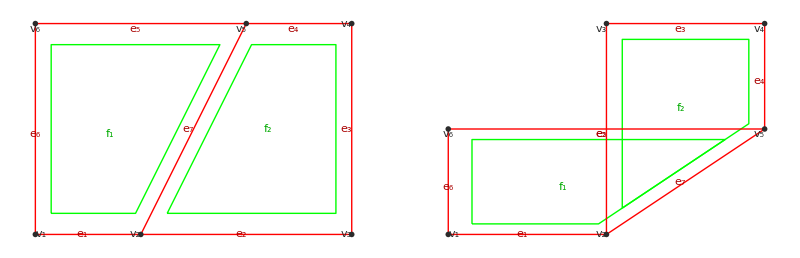

{{2,1}}

```mathematica
Module[{vertscp,vertsff,edges,faces,types,tobjcp,tobjff},
vertscp={{0,0},{1,0},{3,0},{3,1},{2,1},{0,1}};
vertsff={{0,0},{1,0},{1,2},{2,2},{2,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{2,5}};
types={B,B,B,B,B,B,V};
faces={{1,2,5,6},{2,3,4,5}};
tobjcp=MakeTGraphAssigned[vertscp,edges,faces,types];
tobjff=tobjcp//ReplaceProperty[Vertices->vertsff];
Print[GraphicsRow[{GraphGraphics[tobjcp],GraphGraphics[tobjff]}]];
LocalFaceOrdering[tobjcp]
]
```

Example. Make a plane graph, assign it, then calculate the local facet ordering. We’ll visualize the ordering by using GenericGraphGraphics on the face centroids and local facet ordering.

Note: the Combinatorica functions ShowGraph could, in principle, show the ordered graph, but if we want to superimpose the ordering graph on the original graph, we have to do it this way with GenericGraphGraphics because ShowGraph renormalizes the embedding coordinates.

```mathematica
Module[{tobj,fc,fverts,dverts,lfo,fgraph},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
lfo=LocalFaceOrdering[tobj,FaceupFace->1];
GraphicsGrid[{{
GraphGraphics[tobj,FaceColoring->TwoColorGraph[tobj,StartFace->1]],
CreasePatternGraphics[tobj]/.OrigamiStyle[]},{
Graph2DGraphics[tobj],
Show[GraphGraphics[tobj],
GenericGraphGraphics[FaceCentroids[tobj],lfo,{},DirectedEdges->True,EdgeColor->Blue,VertexLabels->None]]}}]
]//ShowExample
```

#### FaceOverlaps2D[tobj] (unchecked class) TGraph2D

FaceOverlaps[tobj] returns a list of undirected edges on the Vertices2D faces that define the overlap graph; an edge {i, j} is in the graph iff the folded form embedding of face i and face j overlap.

You can rely on the ordering of the indices: first index is always smaller.

```mathematica
FaceOverlaps2D[tobj_TObj]:=Module[{verts2d,faces,polys,infos,oedges},
{verts2d,faces}=GetValues[tobj,{Vertices2D,Faces}];
polys=verts2d⟦#⟧&/@faces;
infos=QuasiConvexPolygonIntersectionInfo/@polys; (* each entry is {verts, bbox, convex, triangles } *)
oedges={};
Do[
(* first quick check, see if bounding boxes intersect *)
If[!BoundingBoxesIntersectQ[infos⟦i,2⟧,infos⟦j,2⟧],Continue[]];
(* now check for real *)
If[QuasiConvexPolygonsIntersectQ[infos⟦i⟧,infos⟦j⟧],AppendTo[oedges,{j,i}]];
,{i,2,Length[faces]},{j,i-1}];
oedges]
```

Example.

```mathematica
Module[{tobj,fo},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
fo=FaceOverlaps2D[tobj];
Print[fo];
GraphicsGrid[{{
GraphGraphics[tobj,FaceColoring->TwoColorGraph[tobj,StartFace->1]],
CreasePatternGraphics[tobj]/.OrigamiStyle[]},{
Graph2DGraphics[tobj],
Show[GraphGraphics[tobj],
GenericGraphGraphics[FaceCentroids[tobj],fo,{},EdgeColor->Blue,VertexLabels->None]]}}]
]//ShowExample
```

#### EdgeOverlaps2D[tobj, opts] (unchecked class) TGraph2D (options) IncludeCollinear

EdgeOverlaps2D[tobj] returns a list of undirected edges on the Vertices2D embedding of the edges that define the edge overlap graph; an edge {i, j} is in the overlap graph iff the folded form embedding of edge i and edge j overlap. Options are:
	IncludeCollinear → True | False, is passed thrugh to SegmentsIntersectQ.

You can rely on the ordering of the indices: first index is always smaller.

```mathematica
EdgeOverlaps2D[tobj_TObj,opts___]:=Module[{verts2d,edges,epairs,oedges},
{verts2d,edges}=GetValues[tobj,{Vertices2D,Edges}];
epairs=verts2d⟦#⟧&/@edges;
oedges={};
Do[
(* don't bother with edges that share a vertex *)
If[Or[edges⟦i,1⟧==edges⟦j,1⟧,edges⟦i,1⟧==edges⟦j,2⟧,edges⟦i,2⟧==edges⟦j,1⟧,edges⟦i,2⟧==edges⟦j,2⟧],Continue[]];
(* first quick check, see if bounding boxes intersect *)
If[!BoundingBoxesIntersectQ[BoundingBox[epairs⟦i⟧],BoundingBox[epairs⟦j⟧]],Continue[]];
(* now check for real *)
If[SegmentsIntersectQ[epairs⟦i⟧,epairs⟦j⟧,opts],AppendTo[oedges,{j,i}]];
,{i,2,Length[edges]},{j,i-1}];
oedges]
```

Example.

```mathematica
Module[{tobj,eo},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
eo=EdgeOverlaps2D[tobj];
Print[eo];
GraphicsGrid[{{
GraphGraphics[tobj,FaceColoring->TwoColorGraph[tobj,StartFace->1]],
CreasePatternGraphics[tobj]/.OrigamiStyle[]},{
Graph2DGraphics[tobj,Frame->True],
Show[GraphGraphics[tobj],
GenericGraphGraphics[EdgeCentroids[tobj],eo,{},EdgeColor->Blue,VertexLabels->None]]}}]
]//ShowExample
```

#### EdgeFacePairs[tobj] (unchecked class) TGraph

EdgeFacePairs[tobj] returns a list of the indices of the incident faces for each edge in tobj.

This is the same data that’s in the property EdgeFaceIncidence of a TPlaneGraph, but we don’t require a full TPlaneGraph, since circular polygon graphs and twist tiles are not those; they’re missing their border edges.

```mathematica
EdgeFacePairs[tobj_TObj]:=Module[{edges,faces,fe},
{edges,faces}=GetValues[tobj,{Edges,Faces}];
fe=Join[#,Reverse/@#]&/@(Transpose[{#,RotateLeft[#]}]&/@faces);(* all edges for each face *)
First/@Position[fe,#]&/@edges]
```

Example.

```mathematica
Module[{tobj,efp},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
efp=EdgeFacePairs[tobj];
Print[efp];
GraphGraphics[tobj]
]//ShowExample
```

#### FacesAboveOld[tobj, opts] [deprecated] (options) FaceupFace, MaxDistance, ShowProgress

FacesAboveOld[tobj, opts] takes a list dedges of directed edges on the faces of a crease pattern that defines a local ordering graph on the faces and returns a list where the ith entry in the list is a list of the indices of all the faces that lie above the ith face.

As its (new) name suggests, it is deprecated. We have a new and improved algorithm below.

This uses a heuristic algorithm: it simply returns every face within MaxDistance above the ith face. To get all faces above each face, pass the value MaxDistance→∞.

Note, however, that with cyclic twists, every facet in a cycle lies "above" any one of the facets. The way we break the cycle, which is somewhat heuristic, is that we look for cycles (pairs in the all-pairs-shortest-path matrix that are symmetric about the diagonal) and we assume "shortest path wins"; that is, the shortest path in the cycle describes the proper ordering relationship between the two facets. In case of a tie, we'll assume incomparability.

This is a simple heuristic that does surprisingly well for rendering a plausible folded form. We note, though, something as simple as a VVMVM pentagonal twist tile defeats it.

```mathematica
MaxDistance::usage="MaxDistance is an option to FacesAboveOld that specifies how far away we look for a covering-up face.";
```

```mathematica
Options[FacesAboveOld]={
MaxDistance->∞,
ShowProgress->False,
};
```

```mathematica
FacesAboveOld[tobj_TObj,opts___]:=Module[{md,sp,dedges,nf,apsp,fa,aedges},
md=MaxDistance/.{opts}/.Options[FacesAboveOld];
sp=ShowProgress/.{opts}/.Options[FacesAboveOld];
dedges=LocalFaceOrdering[tobj,opts];
If[sp,
(* show the original local facet ordering graph *)
Print[Show[GraphGraphics[tobj],
GenericGraphGraphics[FaceCentroids[tobj],dedges,{},DirectedEdges->True,EdgeColor->RGBColor[0,.5,1],VertexLabels->None]]];
];
nf=Max[Flatten[dedges]];
(* graph distance matrix *)
apsp=GraphDistanceMatrix[Graph[dedges]];

Do[If[apsp⟦i,j⟧≠∞&&apsp⟦j,i⟧≠∞,
Which[apsp⟦i,j⟧<apsp⟦j,i⟧,apsp⟦j,i⟧=∞,
apsp⟦i,j⟧>apsp⟦j,i⟧,apsp⟦i,j⟧=∞,
True (* apsp⟦i,j⟧==apsp⟦j,i⟧ *),apsp⟦i,j⟧=apsp⟦j,i⟧=∞]],
{i,2,Length[apsp]-1},{j,i+1,Length[apsp]}];
fa=Flatten/@MapIndexed[If[#1≠0&&#1≠∞&&#1≤md,#2⟦2⟧,{}]&,Transpose[apsp],{2}];
If[sp,
(* Show a sequence of graphs showing which faces lie above each face in turn. *)
(* aedges are edges of the "above" graph. {i,j} means i is above j. *)
aedges=First/@MapIndexed[{#1,#2⟦1⟧}&,fa,2];
(* Show which facets lie above each individual facet as a series of graphs *)
Print[GraphicsGrid[Partition[Show[
CreasePatternGraphics[tobj]/.OrigamiStyle[],
GenericGraphGraphics[FaceCentroids[tobj],#,{},DirectedEdges->True,EdgeColor->Red]]&/@aedges,3]]];
];
fa]
```

Example: a non-cyclic twist.

```mathematica
Module[{tobj,fa},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
Print[GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj],Graph2DGraphics[tobj]}]/.OrigamiStyle[]];
fa=FacesAboveOld[tobj,ShowProgress->True];
fa
]//ShowExample
```

Example: a cyclic twist. This will demonstrate the breaking of cycles.

```mathematica
Module[{tobj,fa},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes1];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
Print[GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj],Graph2DGraphics[tobj]}]/.OrigamiStyle[]];
fa=FacesAboveOld[tobj,ShowProgress->True];
fa
]//ShowExample
```

#### FacesAboveAutomatic[tobj, opts] (unchecked classes) TGraph2D+TAssigned (options) ShowProgress, ReportInconsistentOrdering, FaceupFace

FacesAboveAutomatic[tobj, opts] takes a TGraph2D+TAssigned and returns an ordered list of face indices above each face where the ith entry in the list is a list of the indices of all the faces that lie above the ith face.

Options:
	ShowProgress → True | False, if true, display some graphs showing the relationships that are used along the way.
	ReportInconsistentOrdering → True | False, if true, post a Message if an inconsistent ordering was detected.
	FaceupFace → fuface, passed through to LocalFaceOrdering.

In general, this problem is (notoriously) NP-hard. We apply some heuristics that give a good answer for most twist tessellations.

Comment. If two edges overlap collinearly, the ordering condition for the adjacent facets is a bit more complicated, so we don’t consider those (yet).

```mathematica
ReportInconsistentOrdering::usage="ReportInconsistentOrdering is an option to FacesAboveAutomatic that specifies whether to report inconsistent ordering encountered during computation of the folded form.";
```

```mathematica
Options[FacesAboveAutomatic]={
ShowProgress->False,
ReportInconsistentOrdering->True
};
```

```mathematica
FacesAboveAutomatic::incons="Inconsistent face ordering was detected for face pairs `1`.";
```

```mathematica
FacesAboveAutomatic[tobj_TObj,opts___]:=Module[{sp,rio,nf,lfo,lfoold,fo,eo,efp,fa,eofn,eobadf,ei,ej,fi1,fi2,fj1,fj2,m11ij,m12ij,m21ij,m22ij,m11ji,m12ji,m21ji,m22ji,lfog,gdm,fi,fj,plij,plji,aedges},
sp=ShowProgress/.{opts}/.Options[FacesAboveAutomatic];
rio=ReportInconsistentOrdering/.{opts}/.Options[FacesAboveAutomatic];
nf=Length[tobj[Faces]];
fo=FaceOverlaps2D[tobj]; (* undirected edges on the faces that specify overlapping *)
eo=EdgeOverlaps2D[tobj,IncludeCollinear->False];(* undirected edges on the edges that specify overlapping *)
efp=EdgeFacePairs[tobj];(* faces incident to each edge *)
fa=Table[{},{nf}];(* list of faces above faces, to be populated *)
(* start with the local facet ordering from crease directions and 2-coloring *)
lfoold=lfo=LocalFaceOrdering[tobj,opts];(* directed edges on the faces that specify local ordering *)
(* Go through all overlapping edges and if there's an ordering between any two of the incident facets, add that ordering relationship between the other facets *)
eobadf={};(* running tally of face pairs for which contradictory ordering was implied. *)
eofn=Function[e,
{ei,ej}=e;(* indices of edges that overlap *)
If[Length[efp⟦ei⟧]==2&&Length[efp⟦ej⟧]==2,(* both edges incident to 2 facets *)
{fi1,fi2}=efp⟦ei⟧;(* faces incident to ei *)
{fj1,fj2}=efp⟦ej⟧;(* faces incident to ej *)
(* check for existence of {i,j} ordering or {j,i} ordering among any pair of the 4 faces *)
m11ij=MemberQ[lfo,{fi1,fj1}];
m12ij=MemberQ[lfo,{fi1,fj2}];
m21ij=MemberQ[lfo,{fi2,fj1}];
m22ij=MemberQ[lfo,{fi2,fj2}];
m11ji=MemberQ[lfo,{fj1,fi1}];
m12ji=MemberQ[lfo,{fj1,fi2}];
m21ji=MemberQ[lfo,{fj2,fi1}];
m22ji=MemberQ[lfo,{fj2,fi2}];
(* if any ordering exists for one face pair, add the corresponding ordering for the other pairs, but only if the reverse ordering for those pairs does not exist. If a reverse ordering does exist, we've reached an inconsistent state; we won't add the inconsistent ordering to the local face ordering and we'll make a note of the bad ordering. *)
(* check for {i,j} ordering *)
If[Or[m11ij,m12ij,m21ij,m22ij],
If[!m11ij,If[!m11ji,AppendTo[lfo,{fi1,fj1}],AppendTo[eobadf,{fi1,fj1}]]];
If[!m12ij,If[!m12ji,AppendTo[lfo,{fi1,fj2}],AppendTo[eobadf,{fi1,fj2}]]];
If[!m21ij,If[!m21ji,AppendTo[lfo,{fi2,fj1}],AppendTo[eobadf,{fi2,fj1}]]];
If[!m22ij,If[!m22ji,AppendTo[lfo,{fi2,fj2}],AppendTo[eobadf,{fi2,fj2}]]];
];
(* check for {j,i} ordering *)
If[Or[m11ji,m12ji,m21ji,m22ji],
If[!m11ji,If[!m11ij,AppendTo[lfo,{fj1,fi1}],AppendTo[eobadf,{fj1,fi1}]]];
If[!m12ji,If[!m12ij,AppendTo[lfo,{fj1,fi2}],AppendTo[eobadf,{fj1,fi2}]]];
If[!m21ji,If[!m21ij,AppendTo[lfo,{fj2,fi1}],AppendTo[eobadf,{fj2,fi1}]]];
If[!m22ji,If[!m22ij,AppendTo[lfo,{fj2,fi2}],AppendTo[eobadf,{fj2,fi2}]]];
];
]];
(* Repeatedly apply the function to the list of edge overlaps until our list of local facet overlaps no longer changes *)
FixedPoint[Function[x,eofn/@eo;lfo],Null];
eobadf=Union[eobadf];
(* report any inconsistencies *)
If[rio&&!ListEmptyQ[eobadf],
Message[FacesAboveAutomatic::incons,eobadf];
];
If[sp,
(* print and show the old and new local face ordering graphs *)
Print["local ordering = ",lfoold];
Print["extended ordering = ",lfo];
Print[GraphicsRow[{
Show[GraphGraphics[tobj],
GenericGraphGraphics[FaceCentroids[tobj],lfoold,{},DirectedEdges->True,EdgeColor->RGBColor[0,.5,1],VertexLabels->None]],
Show[GraphGraphics[tobj],
GenericGraphGraphics[FaceCentroids[tobj],lfo,{},DirectedEdges->True,EdgeColor->Blue,VertexLabels->None]]}]]];

(* Build a Graph from the lfo edges. We'll query this for path lengths. *)
lfog=Graph[Range[nf],DirectedEdge@@#&/@lfo];
gdm=GraphDistanceMatrix[lfog];
(* gdm⟦i,j⟧ gives the path length for facet i being covered by facet j *)
If[sp,
Print["path length matrix = ",MatrixForm[gdm]]
];
(* Go through overlapping face pairs and try to determine their relative order. If successful, push a face index onto the proper faces-above array. *)
Function[f,
{fi,fj}=f;(* indices of two overlapping faces *)
plij=gdm⟦fi,fj⟧;(* path length for i covered by j *)
plji=gdm⟦fj,fi⟧;(* path length for j covered by i *)
(* path length = 1 means no path exists *)
Which[
plij<plji,AppendTo[fa⟦fj⟧,fi],(* i above j *)
plij>plji,AppendTo[fa⟦fi⟧,fj],(* j above i *)
True,Null(* either no path or same length *)
]]/@fo;
If[sp,
(* Show a sequence of graphs showing which faces lie above each face in turn. *)
(* aedges are edges of the "above" graph. {i,j} means i is above j. *)
aedges=First/@MapIndexed[{#1,#2⟦1⟧}&,fa,2];
(* Show which facets lie above each individual facet as a series of graphs *)
Print[GraphicsGrid[Partition[Show[
CreasePatternGraphics[tobj]/.OrigamiStyle[],
GenericGraphGraphics[FaceCentroids[tobj],#,{},DirectedEdges->True,EdgeColor->Red]]&/@aedges,3]]];
];
fa]
```

Example. A non-cyclic twist.

```mathematica
Module[{tobj,fa},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
Print[GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj],Graph2DGraphics[tobj]}]/.OrigamiStyle[]];
fa=FacesAboveAutomatic[tobj,ShowProgress->True];
fa
]//ShowExample
```

Example. A cyclic twist.

```mathematica
Module[{tobj,fa},
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes1];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[pgtypes],StationaryFace->4];
Print[GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj],Graph2DGraphics[tobj]}]/.OrigamiStyle[]];
fa=FacesAboveAutomatic[tobj,ShowProgress->True];
fa
]//ShowExample
```

#### VisibleFoldedFormLines[tobj, opts] (unchecked classes) TGraph2D+TAssigned (options) FacesAbove, FaceupFace, ShowProgress, ReportInconsistentOrdering, Options[Graphics]

VisibleFoldedFormLines[tobj, opts] takes a TGraph2D+TAssigned and returns a list of folded form lines in which visible and covered lines are rendered so that visible folded lines are rendered with style FoldedLine, visible border lines are rendered with style BorderLine,  and hidden folded and border lines are rendered with style HiddenFoldedLine.

Options:
	FacesAbove → fa | Automatic, where fa is a list of of the face indices that lie above each face. Automatic means we calculate it using our own algorithm, which will make use of FaceupFace, see next.
	FaceupFace → fuface specifies a face-up face if we have to calculate our own facet ordering.
	ShowProgress → True | False, if true, display some graphs showing the relationships that are used along the way.
	ReportInconsistentOrdering → True | False, if true, post a Message if an inconsistent ordering was detected; passed through to FacesAboveAutomatic (if used).
	Options[Graphics] are passed through.

```mathematica
FacesAbove::usage="FacesAbove is an option to VisibleFoldedFormLines that specifies whether to calculate facet ordering from local ordering or to provide an explicit list of indices of faces lying about each face.";
```

```mathematica
Options[VisibleFoldedFormLines]={
FacesAbove->Automatic,
FaceupFace->1,
ShowProgress->False
};
```

```mathematica
VisibleFoldedFormLines[tobj_TObj, opts___]:=Module[{fa,ff,sp,verts,verts2d,edges,types,faces,fverts,dedges,aedges,tm,epfi,trules,emap,ss,cpolys,ssl1,ssl2},
fa=FacesAbove/.{opts}/.Options[VisibleFoldedFormLines];ff=FaceupFace/.{opts}/.Options[VisibleFoldedFormLines];sp=ShowProgress/.{opts}/.Options[VisibleFoldedFormLines];
{verts,verts2d,edges,types,faces}=GetValues[tobj,{Vertices,Vertices2D,Edges,EdgeTypes,Faces}];
If[sp,fverts=FaceCentroids[tobj]]; (* need these for various progress graphs *)
dedges=LocalFaceOrdering[tobj,opts]; (* used to construct emap *)
fa=FacesAboveAutomatic[tobj,opts];(* try our new version! *)
(* trules maps an edge index pair (either order) to its type *)
trules=Join[MapThread[Rule,{edges,types}],MapThread[Rule,{Reverse/@edges,types}]];
(* epfi is a list of the edge pair vertex and face incidences, i.e., {{vi, vj},{fk,fl}} for each edge. *)
tm=(Sort/@Transpose[{#,RotateLeft[#]}])&/@faces;
epfi={#,Transpose[Position[tm,#]]⟦1⟧}&/@Union[Flatten[tm,1]];
(* emap will be a table listing each edge, a list of all faces that lie above it, and its type *)
emap={
#⟦1⟧,(* the edge itself *)
If[Length[#⟦2⟧]==1,
fa⟦#⟦2,1⟧⟧,(* face incident to a border edge *)
fa⟦If[MemberQ[dedges,#⟦2⟧],#⟦2,1⟧,#⟦2,2⟧]⟧ (* use the upper face incident to this edge *)
],
#⟦1⟧/.trules (* the type of this edge *)
}&/@epfi;
(* delete any edges that we couldn't assign a type to, which would typically arise if the tobj was missing edges (e.g., is borderless). *)
emap=Select[emap,Length[#⟦3⟧]≠2&];
(* convert each entry in this map to a list of segment sets and then to styled lines *)
Flatten[Function[ee,
ss=Append[verts2d⟦ee⟦1⟧⟧,{{0,1}}];
cpolys=verts2d⟦faces⟦#⟧⟧&/@ee⟦2⟧;
ss=Chop[Fold[ClipSegmentSetToQuasiConvexPolygonExterior[#1,#2]&,ss,cpolys]];
{ssl1,ssl2}=SegmentSetLines[ss];
{If[ListEmptyQ[ssl1],{},Style[ssl1,ee⟦3⟧/.TypeToVisibleFoldedFormStyleRules]],
If[ListEmptyQ[ssl2],{},Style[ssl2,ee⟦3⟧/.TypeToHiddenFoldedFormStyleRules]]}
]/@emap]]
```

Example. A single fold. Note that by changing the FaceupFace to the opposite parity, we effectively reverse the stacking order of the facets.

```mathematica
Module[{vertscp,vertsff,edges,faces,types,tobj},
vertscp={{0,0},{1,0},{3,0},{3,1},{2,1},{0,1}};
vertsff={{0,0},{1,0},{1,2},{2,2},{2,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{2,5}};
types={B,B,B,B,B,B,V};
faces={{1,2,5,6},{2,3,4,5}};
tobj=MakeTGraph2DAssigned[vertscp,edges,faces,vertsff,types];
Print["Local facet ordering = ",LocalFaceOrdering[tobj]];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj],
CreasePatternGraphics[tobj],
Graphics[VisibleFoldedFormLines[tobj]],
Graphics[VisibleFoldedFormLines[tobj,FaceupFace->-1]]
}]/.OrigamiStyle[]
]//ShowExample
```

Example. A twist.

```mathematica
Module[{tobj,fc,lfo,gfa},
(* crease pattern *)
tobj=MakeTPlaneGraph[pgvertscp,pgedges,pgfaces]//AddTAssigned[pgtypes];
(* primal-dual showing ordering *)
tobj=tobj//AddTPrimalDualGraph;
lfo=LocalFaceOrdering[tobj,FaceupFace->1];
tobj=tobj//ReplaceProperty[DualEdges->lfo];
(* two-colored graph *)
fc=TwoColorGraph[tobj,StartFace->1];
(* folded form *)
tobj=tobj//AddTGraph2D[pgvertsff];
(* output *)
Print["edge/type pairs = ",Transpose[{Range[Length[tobj[Edges]]],tobj[EdgeTypes]}]];
GraphicsRow[{
GraphGraphics[tobj,FaceColoring->fc],
CreasePatternGraphics[tobj],
PrimalDualGraphics[tobj,DualDirectedEdges->True],
Graphics[{StdVertexLabels[pgvertsff],VisibleFoldedFormLines[tobj]}]
}]/.OrigamiStyle[]
]//ShowExample
```

#### VisibleFoldedFormGraphics[tobj, opts] (checked classes) TGraph2D+TAssigned (options) PaperFill, FacesAbove, FaceupFace, ShowProgress, ReportInconsistentOrdering, Options[Graphics]

VisibleFoldedFormGraphics[tobj, opts] takes a TGraph2D+TAssigned and returns a rendering of both lines and polygons in the folded form in which visible and covered lines are rendered so that visible folded lines are rendered with style FoldedLine, visible border lines are rendered with style BorderLine,  and hidden folded and border lines are rendered with style HiddenFoldedLine.

Options:
	PaperFill → PaperWhiteSideFill | PaperColoredSideFill, specifies the color of the paper that will be used to render all polygons.	
	FacesAbove → fa | Automatic, where fa is a list of of the face indices that lie above each face. Automatic means we calculate it using our own algorithm, which will make use of FaceupFace, see next.
	FaceupFace → fuface specifies a face-up face if we have to calculate our own facet ordering.
	ShowProgress → True | False, if true, display some graphs showing the relationships that are used along the way.
	ReportInconsistentOrdering → True | False, if true, post a Message if an inconsistent ordering was detected; passed through to FacesAboveAutomatic (if used).
	Options[Graphics] are passed through.

Note that by switching the FaceupFace to a face of the opposite parity and flopping the folded form using FlopGraph2D, you can effectively “turn over” the folded form.

```mathematica
VisibleFoldedFormGraphics[tobj_TObj, opts___]:=Module[{},
AssertClasses[tobj,{TGraph2D,TAssigned},VisibleFoldedFormGraphics];
Graphics[
{FoldedFormPolys[tobj,opts],
VisibleFoldedFormLines[tobj,opts]},FilterRules[{opts},Options[Graphics]]]]
```

Example. A single fold.

```mathematica
Module[{vertscp,vertsff,edges,faces,types,tobj},
vertscp={{0,0},{1,0},{3,0},{3,1},{2,1},{0,1}};
vertsff={{0,0},{1,0},{1,2},{2,2},{2,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{2,5}};
types={B,B,B,B,B,B,V};
faces={{1,2,5,6},{2,3,4,5}};
tobj=MakeTGraph2DAssigned[vertscp,edges,faces,vertsff,types];
Print["Local facet ordering = ",LocalFaceOrdering[tobj]];
GraphicsRow[{
GraphGraphics[tobj],
Graph2DGraphics[tobj],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj],
VisibleFoldedFormGraphics[FlopGraph2D[tobj],FaceupFace->2]}]/.OrigamiStyle[]
]//ShowExample
```

Example. This compares 3 ways of rendering the same folded form twist, depending on what you want to show off.

```mathematica
Module[{},
GraphicsRow[{
CreasePatternGraphics[pgtobj],(* crease pattern showing direction of the folds *)
GenericFoldedFormGraphics[pgtobj], (* generic rendering, all fold lines are hidden *)
VisibleFoldedFormGraphics[pgtobj](* hidden line removal *)
}]/.OrigamiStyle[]
]//ShowExample
```

This example compares rendering of three different twists using visible folded form.

```mathematica
Module[{},
GraphicsGrid[Transpose[{
{CreasePatternGraphics[pgtobj],VisibleFoldedFormGraphics[pgtobj]},
{CreasePatternGraphics[pgtobj1],VisibleFoldedFormGraphics[pgtobj1]},
{CreasePatternGraphics[pgtobj2],VisibleFoldedFormGraphics[pgtobj2]}
}]]/.OrigamiStyle[]
]//ShowExample
```

This shows details of the rendering of a pentagon twist that confounded the old VisibleFoldedFormGraphics routine.

```mathematica
Module[{vertscp,vertsff,edges,types,faces,tobj,pg,cp,ff},
{vertscp,vertsff,edges,types,faces}={{{0.7212601477285518,0.606300738642759},{0.6,0.},{1.123606797749979,0.3804226065180615},{0.6462553746927469,0.8733163953839403},{0.3691306448689169,0.8844949929322115},{0.823606797749979,1.3037276676706375},{0.17639320225002098,1.3037276676706375},{0.27286291575046334,0.624388089422418},{0.490490916959321,0.45245458479660516},{-0.12360679774997896,0.3804226065180615},{0.4,0.},{1.1854101966249684,0.5706339097770922},{0.9854101966249684,1.186170617212143},{0.014589803375031574,1.186170617212143},{-0.1854101966249685,0.5706339097770922},{1.,2.7755575615628914*^-17},{1.3090169943749475,0.9510565162951538},{0.5,1.538841768587627},{-0.30901699437494745,0.9510565162951535},{0.,0.}},{{0.7212601477285518,0.606300738642759},{0.6,0.},{1.123606797749979,0.3804226065180615},{0.45424449098737063,0.5312959656069538},{0.4430658934390996,0.25417123578312384},{0.8975420463201613,0.6734039105215504},{0.2503284508202035,0.6734039105215498},{0.7031727969488931,0.15790350666467057},{0.8751063015747056,0.3755315078735282},{0.2610085868654055,0.30349952959498483},{0.7846153846153846,-0.07692307692307698},{0.9933993129195924,0.22861348000010612},{0.7933993129195919,0.8441501874351567},{0.44489968457346074,0.7196860344543949},{0.24489968457346079,0.10414932701934498},{1.,2.7755575615628914*^-17},{1.1170061106695712,0.6090360865181679},{0.5739352485701824,0.9085180114385396},{0.12129288682348194,0.48457193353740635},{0.38461538461538447,-0.07692307692307676}},{{1,2},{3,1},{1,4},{5,6},{7,5},{5,8},{9,10},{11,9},{9,1},{4,12},{13,4},{4,5},{8,14},{15,8},{8,9},{11,2},{3,12},{13,6},{7,14},{15,10},{2,16},{16,3},{12,17},{17,13},{6,18},{18,7},{14,19},{19,15},{10,20},{20,11}},{M,M,M,M,M,M,M,V,V,V,V,V,V,V,V,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B},{{1,2,16,3},{1,4,5,8,9},{5,6,18,7},{9,10,20,11},{4,12,17,13},{8,14,19,15},{11,2,1,9},{3,12,4,1},{13,6,5,4},{7,14,8,5},{15,10,9,8}}};
tobj=MakeTGraph2DAssigned[vertscp,edges,faces,vertsff,types];
pg=GraphGraphics[tobj];
cp=CreasePatternGraphics[tobj];
ff=VisibleFoldedFormGraphics[tobj,ShowProgress->True];
GraphicsRow[{pg,cp,ff}/.OrigamiStyle[]]
]//ShowExample
```

### TGraph2D+TAssigned rendered crease pattern/folded form pairs

#### GenericPairGraphics[tobj, opts] (checked classes) TGraph2D+TAssigned (options) Spacing, PaperFill, Options[Graphics] VisiblePairGraphics[tobj, opts] (checked class) TGraph2D+TAssigned (options) Spacing, PaperFill, FacesAbove, FaceupFace, ShowProgress, Options[Graphics]

GenericPairGraphics[tobj, opts] takes a TGraph2D+TAssigned representing the crease pattern and the folded form and returns a single Graphics object that displays both the crease pattern and generic folded form side-by-side, with the crease pattern centered on the x-axis about the origin. Options are:
	Spacing → r, where r is the fractional width by which to space the two objections, passed through to PlaceInRowGraphics.
	PaperFill → PaperWhiteSideFill | PaperColoredSideFill, specifies the color of the paper that will be used to render all polygons, passed through to FoldedFormPolys.
	Options[Graphics] are passed through.

A reason for using this function rather than a GraphicsRow containing the two individual Graphics objects is that this function will display the two patterns at the same relative scale.

```mathematica
CreasePatternGraphics[pgtobj]/.OrigamiStyle[]
```

CreasePatternGraphics[pgtobj]

```mathematica
GenericPairGraphics[tobj_TObj, opts___]:=Module[{},
AssertClasses[tobj,{TGraph2D,TAssigned},GenericPairGraphics];
Graphics[PlaceInRowGraphics[{
CreasePatternGraphics[tobj,opts],
GenericFoldedFormGraphics[tobj,opts]},opts]⟦1⟧,FilterRules[{opts},Options[Graphics]]]]
```

Example

```mathematica
GenericPairGraphics[pgtobj,Frame->True]/.OrigamiStyle[]//ShowExample
```

VisiblePairGraphics[tobj, opts] takes a TGraph2D+TAssigned representing the crease pattern and the folded form, and returns a single Graphics object that displays both the crease pattern and hidden-line-removed folded form side-by-side, centered on the x-axis about the origin. Options are:
	Spacing→r, where r is the fractional width by which to space the two objections.
	PaperFill → PaperWhiteSideFill | PaperColoredSideFill, specifies the color of the paper that will be used to render all polygons.	
	FacesAbove → fa | Automatic, where fa is a list of of the face indices that lie above each face. Automatic means we calculate it using our own algorithm, which will make use of FaceupFace, see next.
	FaceupFace → fuface specifies a face-up face if we have to calculate our own facet ordering.
	ShowProgress → True | False, if true, display some graphs showing the relationships that are used along the way.
	Options[Graphics] are passed through.

```mathematica
VisiblePairGraphics[tobj_TObj,opts___]:=Module[{},
AssertClasses[tobj,{TGraph,TAssigned},VisiblePairGraphics];
Graphics[PlaceInRowGraphics[{CreasePatternGraphics[tobj,opts],VisibleFoldedFormGraphics[tobj,opts]}]⟦1⟧,FilterRules[{opts},Options[Graphics]]]]
```

Example

```mathematica
VisiblePairGraphics[pgtobj,Frame->True]/.OrigamiStyle[]//ShowExample
```

### Class TPlaneGraphAssigned

#### Notes

Class TPlaneGraphAssigned is a convenience class useful for adding an assignment to a TPlaneGraph when we don’t need an embedding of the folded form.

This class is provided as a convenience since the combination of TPlaneGraph and TAssigned happens regularly.

Note that functions that require both assignment and plane graphs will check for the individual classes TPlaneGraph and TGraphAssigned; they’ll work if both subclasses are present, even if the passed object isn’t specifically an TPlaneGraphAssigned.

#### TObj class: TPlaneGraphAssigned Inherits from: TPlaneGraph, TAssigned

TPlaneGraphAssigned is a TObj class that represents a full plane graph with crease assignment on its edges.

```mathematica
TPlaneGraphAssigned::usage="TPlaneGraphAssigned is a TObj class that represents a full plane graph with crease assignment on its edges.";
```

```mathematica
RegisterTClass[TPlaneGraphAssigned,{TPlaneGraph,TAssigned}];
```

#### MakeTPlaneGraphAssigned[verts, edges] MakeTPlaneGraphAssigned[verts, edges, faces] MakeTPlaneGraphAssigned[verts, edges, faces, types]

As with all convenience classes, TPlaneGraphAssigned has only Make constructors.

MakeTPlaneGraphAssigned[verts, edges, faces, types] creates a TPlaneGraphAssigned from its constitutent parts.

```mathematica
MakeTPlaneGraphAssigned[verts_List, edges_List, faces_List:{},types_List:{}]:=
MakeTPlaneGraph[verts,edges,faces]//AddTAssigned[If[ListEmptyQ[types],Table[U,{Length[edges]}],types]]//AddClass[TPlaneGraphAssigned]
```

Example

```mathematica
Module[{verts,edges,faces,types,tobj},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
faces={{1,2,3,4}};
types={M,M,V,V};
tobj=MakeTPlaneGraphAssigned[verts,edges,faces,types];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### Converting from crease pattern to TPlaneGraphAssigned

#### Notes

These functions take symbolically styled crease patterns and convert them to crease-assigned plane graphs. The utility in doing this is that if we have the crease-assigned plane graph of a pattern, we can compute its folded form and (a good approximation of) its visible folded form, thus saving one from the trouble of having to compute both in the design phase.

You can also use this to import a drawn crease pattern to subsequently compute its visible folded form (assuming the crease pattern is drawn accurately and satisfies Kawasaki-Justin).

Note that if you have fold angle indicated by graphical style, you should use CreasePatternToGraph3DAssigned, see below.

If you have both 2D and 3D vertex information, you can add the 3D information using OrderMappingByVertices, see below.

#### CreasePatternStyleToEdgeTypeRules

CreasePatternStyleToEdgeTypeRules provides the mapping from {MountainLine, ValleyLine, UnfoldedLine, BorderLine} back to edge type codes {M,V,U,B}.

```mathematica
CreasePatternStyleToEdgeTypeRules={
MountainLine->M,
ValleyLine->V,
UnfoldedLine->U,
BorderLine->B
};
```

#### CreasePatternToPlaneGraphAssigned[cp, opts] (options) SamePtTolerance, BorderOverride

CreasePatternToPlaneGraphAssigned[cp, opts] takes a list of Line segments styled with some combination of the four crease pattern line types: MountainLine, ValleyLine, UnfoldedLine, BorderLine) and extracts and returns a crease-assigned plane graph description, TPlaneGraphAssigned. Note that if BorderOverride → True, whatever line style you assigned to the border lines, they will be given edge type B. Options are:
	SamePtTolerance → tol, where tol is the tolerance on distance used when the vertices are Indexified.
	BorderOverride → True | False, where True overrides whatever you've set the border lines to and sets them to edge type B.

Note that when you import a file, you should perform style conversion (using ExtractStyleArgs and ReplaceStyleArgs) to apply our symbolic styles *before* you apply CreasePatternToPlaneGraphAssigned.

```mathematica
BorderOverride::usage="BorderOverride is an option to CreasePatternToPlaneGraphAssigned that overrides any fold line assignments on the border lines, setting them to B.";
```

```mathematica
Options[CreasePatternToPlaneGraphAssigned]={
SamePtTolerance->10^-6,
BorderOverride->False
};
```

```mathematica
CreasePatternToPlaneGraphAssigned::badstyles="The styles in this object, `1`, contain more than just {{MountainLine}, {ValleyLine}, {UnfoldedLine}, {BorderLine}}.";
```

```mathematica
CreasePatternToPlaneGraphAssigned::dupvert="The extracted edges `1` contain at least one edge with duplicate vertices `2`.";
```

```mathematica
CreasePatternToPlaneGraphAssigned[cp_,opts___]:=Module[{tol,bo,llist,styles,elist,edgetypes,verts,edges,tobj,faces,boundary,bedges},
tol=SamePtTolerance/.{opts}/.Options[CreasePatternToPlaneGraphAssigned];
bo=BorderOverride/.{opts}/.Options[CreasePatternToPlaneGraphAssigned];
llist=ExtractFracturedStyledLines[cp];
styles=ExtractStyleArgs[llist];
If[Length[Union[styles,{{MountainLine},{ValleyLine},{UnfoldedLine},{BorderLine}}]]>4,Message[CreasePatternToPlaneGraphAssigned::badstyles,styles];Abort[]];
{elist,edgetypes}=Transpose[llist/.Style->List];
edgetypes=edgetypes/.CreasePatternStyleToEdgeTypeRules;
{verts,edges}=Indexify[First/@elist,2,SamePtTolerance->tol];
If[!Union[Length/@Union/@edges]==={2},Message[CreasePatternToPlaneGraphAssigned::dupvert,edges,verts]];
tobj=MakeTGraph[verts,edges]//AddTPlaneGraphTo;
{faces,boundary}=GetValues[tobj,{Faces,BoundaryVertices}];
If[bo,
bedges=Join@@({#,Reverse/@#}&@Transpose[{boundary,RotateLeft[boundary]}]);(* all possible border edges *)
edgetypes=If[MemberQ[bedges,#⟦1⟧],B,#⟦2⟧]&/@Transpose[{edges,edgetypes}]
];
tobj//AddTAssigned[edgetypes]
]
```

Example. This starts with a Graphics crease pattern, turns it into a TPlaneGraphAssigned, then uses that to display it back as a crease pattern again.

```mathematica
Module[{cp,tobj,pg,cp1},
cp=CreasePatternGraphics[pgtobj];
tobj=CreasePatternToPlaneGraphAssigned[cp];
pg=GraphGraphics[tobj];
cp1=CreasePatternGraphics[tobj,PaperFill->PaperColoredSideFill];
GraphicsRow[{cp,pg,cp1}]/.OrigamiStyle[]
]//ShowExample
```

#### CreasePatternToGraph2DAssigned[cp, opts] (options) SamePtTolerance, BorderOverride, StationaryFace

CreasePatternToGraph2DAssigned[cp, opts] takes a crease pattern cp, given as a collection of styled lines and polygons, and turns it into a TGraph2D+TAssigned, i.e., a TGraph representing both crease pattern and folded form. Options are:
	SamePtTolerance → tol, specifies the tolerance to use in Indexification of the vertex coordinates.
	BorderOverride → True | False, where True overrides whatever you’ve set the border lines to and sets them to edge type B.
	StationaryFace → sf, specifies which face remains stationary in the folded form.

```mathematica
CreasePatternToGraph2DAssigned[cp_, opts___]:=Module[{tobj},
tobj=CreasePatternToPlaneGraphAssigned[cp,opts];
FoldGraph2D[tobj,TypeToFlatFoldAngle[tobj[EdgeTypes]],opts]]
```

Example. From a crease pattern to the folded form.

```mathematica
Module[{cp,tobj},
cp=Graphics[{Style[Line[{{59.244, 11.934}, {128.40800000000002, 46.521}}], ValleyLine], Style[Line[{{59.375, 12.068}, {48.648, 1.3453}}], ValleyLine], Style[Line[{{128.412, 46.524}, {63.878, 89.13}}], ValleyLine], Style[Line[{{128.231, 46.571}, {155.678, 39.212}}], ValleyLine], Style[Line[{{63.872, 89.13199999999999}, {59.242000000000004, 11.940999999999999}}], ValleyLine], Style[Line[{{63.922000000000004, 88.952}, {60., 103.603}}], ValleyLine], Style[Line[{{160.312, 116.40700000000001}, {91.14800000000001, 81.822}}], MountainLine], Style[Line[{{160.181, 116.27400000000002}, {170.90800000000002, 126.99600000000001}}], MountainLine], Style[Line[{{91.144, 81.81800000000001}, {155.678, 39.21200000000001}}], MountainLine], Style[Line[{{91.325, 81.77100000000002}, {63.879000000000005, 89.13000000000001}}], MountainLine], Style[Line[{{155.684, 39.210000000000015}, {160.314, 116.4}}], MountainLine], Style[Line[{{155.634, 39.38900000000002}, {159.55599999999998, 24.738000000000017}}], MountainLine], Style[Line[{{0.83743, 1.2787}, {48.24343, 1.2665}}], BorderLine], Style[Line[{{48.27543, 1.2665}, {82.99943, 1.2562}}], BorderLine], Style[Line[{{83.01543000000001, 1.2562}, {145.91843, 1.2403}}], BorderLine], Style[Line[{{0.8374300000000261, 1.2787}, {42.38743000000002, 73.27170000000001}}], BorderLine], Style[Line[{{42.41843000000002, 73.27170000000001}, {59.87043000000002, 103.5417}}], BorderLine], Style[Line[{{59.88543000000002, 103.5417}, {73.40643000000001, 126.99870000000001}}], BorderLine], Style[Line[{{135.76343, 126.99870000000001}, {73.40643, 126.99870000000001}}], BorderLine], Style[Line[{{218.608, 126.998}, {170.499, 126.998}}], BorderLine], Style[Line[{{170.515, 126.998}, {135.74899999999997, 126.99900000000001}}], BorderLine], Style[Line[{{218.592, 126.998}, {176.96, 54.87100000000001}}], BorderLine], Style[Line[{{176.991, 54.872}, {159.67200000000003, 24.898}}], BorderLine], Style[Line[{{159.68800000000002, 24.898}, {146.06300000000002, 1.3230000000000004}}], BorderLine], Style[Line[{{160.312, 116.405}, {176.76, 55.021}}], ValleyLine], Style[Line[{{91.144, 81.818}, {136.08, 126.755}}], ValleyLine], Style[Line[{{59.243, 11.936}, {42.795, 73.32}}], MountainLine], Style[Line[{{128.411, 46.522999999999996}, {83.475, 1.5859999999999985}}], MountainLine]}];
tobj=CreasePatternToGraph2DAssigned[cp,SamePtTolerance->5,StationaryFace->8];
GraphicsRow[{CreasePatternGraphics[tobj],VisibleFoldedFormGraphics[tobj,FaceupFace->8]}]/.OrigamiStyle[]
]//ShowExample
```

#### BorderlessCreasePatternToPlaneGraphAssigned[blcp, opts] [deprecated] (options) SamePtTolerance

This takes a crease pattern with no border and creates a TPlaneGraph+TAssigned from it.

It is now deprecated [no longer used]. In general, you should avoid using borderless graphs; instead, use a bordered graph and don’t display the border edges.

```mathematica
Options[BorderlessCreasePatternToPlaneGraphAssigned]={
	SamePtTolerance->10^-6
};
```

```mathematica
BorderlessCreasePatternToPlaneGraphAssigned::nostyle="The input pattern had no lines with style MountainLine or ValleyLine.";
```

```mathematica
BorderlessCreasePatternToPlaneGraphAssigned::nopolys="The input pattern had no styled polygons so no border could be computed.";
```

```mathematica
BorderlessCreasePatternToPlaneGraphAssigned::badborder="The computed border does not appear to be a single closed loop.";
```

```mathematica
BorderlessCreasePatternToPlaneGraphAssigned::badmerge="The number of merged edges doesn't match the number of merge vertices, possibly because a merge vertex is incident to both mountain and valley folds.";
```

```mathematica
BorderlessCreasePatternToPlaneGraphAssigned[blcp_,opts___]:=Module[{tol,mlines,vlines,spolys,verts,imlines,ivlines,ispolys,medges,vedges,bedges,border,d2vs,medges1,vedges1,medges2,vedges2,edges,edgetypes,vkeep,vmap},
tol=SamePtTolerance/.{opts}/.Options[BorderlessCreasePatternToPlaneGraphAssigned];
(* Start by extracting mountain and valley lines and polys. All else will be ignored. *)
mlines=Cases[blcp,Style[_Line,MountainLine],∞];
vlines=Cases[blcp,Style[_Line,ValleyLine],∞];
spolys=Cases[blcp,Style[_Polygon,___],∞];
If[Length[mlines]+Length[vlines]==0,Message[BorderlessCreasePatternToPlaneGraphAssigned::nostyle];Abort[]];
If[Length[spolys]==0,Message[BorderlessCreasePatternToPlaneGraphAssigned::nopolys];Abort[]];
(* Indexify everything *)
{verts,{imlines,ivlines,ispolys}}=Indexify[{mlines,vlines,spolys},5,SamePtTolerance->tol];
medges=#⟦1,1⟧&/@imlines;(* index pairs for mountain lines *)
vedges=#⟦1,1⟧&/@ivlines;(* index pairs for valley lines *)
bedges=Flatten[Transpose[{#,RotateLeft[#]}]&/@(#⟦1,1⟧&/@ispolys),1];(* all possible polygon index pairs *)
bedges=First/@Select[Tally[bedges,#1==#2||#1==Reverse[#2]&],#⟦2⟧==1&];(* filter to edges with multiplicity 1 *)
If[Or@@(#⟦2⟧≠2&/@Tally[Flatten[bedges]]),Message[BorderlessCreasePatternToPlaneGraphAssigned::badborder];Abort[]];
(* get ordered list of border vertices. *)
border=GetValue[AddTPlaneGraphTo[MakeTGraph[verts,bedges]],BoundaryVertices];
(* find verts with multiplicity=2; those need to be merged *)
d2vs=First/@Select[Tally[Flatten[{medges,vedges}]],#⟦2⟧==2&];
medges1=Select[medges,!IntersectsQ[#,d2vs]&];(* don't need merging *)
vedges1=Select[vedges,!IntersectsQ[#,d2vs]&];(* don't need merging *)
medges2=Select[medges,IntersectsQ[#,d2vs]&];(* needs merging *)
medges2=Select[Function[i,Select[Flatten[Select[medges2,MemberQ[#,i]&]],#≠i&]]/@d2vs,NotListEmptyQ];(* merged *)
vedges2=Select[vedges,IntersectsQ[#,d2vs]&];(* needs merging *)
vedges2=Select[Function[i,Select[Flatten[Select[vedges2,MemberQ[#,i]&]],#≠i&]]/@d2vs,NotListEmptyQ];(* merged *)
If[Length[d2vs]≠Length[medges2]+Length[vedges2],Message[BorderlessCreasePatternToPlaneGraphAssigned::badmerge];Abort[]];
edges=Join[medges1,medges2,vedges1,vedges2,bedges];
edgetypes=Join[Table[M,{Length[medges1]+Length[medges2]}],Table[V,{Length[vedges1]+Length[vedges2]}],Table[B,{Length[bedges]}]];
(* we may still have orphan vertices that got merged out of the graph. So we need to
eliminate the orphan vertices and then renumber the indices in the edges appropriately. *)
vkeep=Union[Flatten[edges]];(* indices of vertices to keep *)
vmap=MapThread[Rule,{Join[vkeep,Table[0,{Length[verts]-Length[vkeep]}]],Range[Length[verts]]}];(* map from old vertex numbers to new ones *)
(* and finally we can rebuild the plane graph *)
MakeTGraph[verts⟦vkeep⟧,edges/.vmap]//AddTPlaneGraphTo//AddTAssigned[edgetypes]
]
```

Example. The test example is composed of two side-by-side unbordered tiles; we merge them into a single CP.

Note that now tessellation tiles have borders, so this configuration is no longer relevant.

```mathematica
Module[{cp,tobj,cp1},
cp=Graphics[{{{Style[Polygon[{{0.48086077196920557,0.2334249423165088},{0.7665750576834912,0.48086077196920557},{0.5191392280307945,0.7665750576834912},{0.2334249423165088,0.5191392280307945}}],PaperWhiteSideFill],Style[Polygon[{{0.4,0.},{0.6,0.},{0.7665750576834912,0.48086077196920557},{0.48086077196920557,0.2334249423165088}}],PaperWhiteSideFill],Style[Polygon[{{1.,0.4},{1.,0.6},{0.5191392280307945,0.7665750576834912},{0.7665750576834912,0.48086077196920557}}],PaperWhiteSideFill],Style[Polygon[{{0.6,1.},{0.4,1.},{0.2334249423165088,0.5191392280307945},{0.5191392280307945,0.7665750576834912}}],PaperWhiteSideFill],Style[Polygon[{{0.,0.6},{0.,0.4},{0.48086077196920557,0.2334249423165088},{0.2334249423165088,0.5191392280307945}}],PaperWhiteSideFill],Style[Polygon[{{0.6,0.},{1.,0.},{1.,0.4},{0.7665750576834912,0.48086077196920557}}],PaperWhiteSideFill],Style[Polygon[{{1.,0.6},{1.,1.},{0.6,1.},{0.5191392280307945,0.7665750576834912}}],PaperWhiteSideFill],Style[Polygon[{{0.4,1.},{0.,1.},{0.,0.6},{0.2334249423165088,0.5191392280307945}}],PaperWhiteSideFill],Style[Polygon[{{0.,0.4},{0.,0.},{0.4,0.},{0.48086077196920557,0.2334249423165088}}],PaperWhiteSideFill]},{Style[Line[{{0.4,0.},{0.48086077196920557,0.2334249423165088}}],ValleyLine],Style[Line[{{0.48086077196920557,0.2334249423165088},{0.7665750576834912,0.48086077196920557}}],ValleyLine],Style[Line[{{0.7665750576834912,0.48086077196920557},{0.6,0.}}],MountainLine],Style[Line[{{1.,0.4},{0.7665750576834912,0.48086077196920557}}],ValleyLine],Style[Line[{{0.7665750576834912,0.48086077196920557},{0.5191392280307945,0.7665750576834912}}],ValleyLine],Style[Line[{{0.5191392280307945,0.7665750576834912},{1.,0.6}}],MountainLine],Style[Line[{{0.6,1.},{0.5191392280307945,0.7665750576834912}}],MountainLine],Style[Line[{{0.5191392280307945,0.7665750576834912},{0.2334249423165088,0.5191392280307945}}],MountainLine],Style[Line[{{0.2334249423165088,0.5191392280307945},{0.4,1.}}],ValleyLine],Style[Line[{{0.,0.6},{0.2334249423165088,0.5191392280307945}}],MountainLine],Style[Line[{{0.2334249423165088,0.5191392280307945},{0.48086077196920557,0.2334249423165088}}],MountainLine],Style[Line[{{0.48086077196920557,0.2334249423165088},{0.,0.4}}],ValleyLine]}},{{Style[Polygon[{{1.4808607719692055,0.2334249423165088},{1.7665750576834913,0.48086077196920557},{1.5191392280307945,0.7665750576834912},{1.2334249423165087,0.5191392280307945}}],PaperWhiteSideFill],Style[Polygon[{{1.4,0.},{1.6,0.},{1.7665750576834913,0.48086077196920557},{1.4808607719692055,0.2334249423165088}}],PaperWhiteSideFill],Style[Polygon[{{2.,0.4},{2.,0.6},{1.5191392280307945,0.7665750576834912},{1.7665750576834913,0.48086077196920557}}],PaperWhiteSideFill],Style[Polygon[{{1.6,1.},{1.4,1.},{1.2334249423165087,0.5191392280307945},{1.5191392280307945,0.7665750576834912}}],PaperWhiteSideFill],Style[Polygon[{{1.,0.6},{1.,0.4},{1.4808607719692055,0.2334249423165088},{1.2334249423165087,0.5191392280307945}}],PaperWhiteSideFill],Style[Polygon[{{1.6,0.},{2.,0.},{2.,0.4},{1.7665750576834913,0.48086077196920557}}],PaperWhiteSideFill],Style[Polygon[{{2.,0.6},{2.,1.},{1.6,1.},{1.5191392280307945,0.7665750576834912}}],PaperWhiteSideFill],Style[Polygon[{{1.4,1.},{1.,1.},{1.,0.6},{1.2334249423165087,0.5191392280307945}}],PaperWhiteSideFill],Style[Polygon[{{1.,0.4},{1.,0.},{1.4,0.},{1.4808607719692055,0.2334249423165088}}],PaperWhiteSideFill]},{Style[Line[{{1.4,0.},{1.4808607719692055,0.2334249423165088}}],ValleyLine],Style[Line[{{1.4808607719692055,0.2334249423165088},{1.7665750576834913,0.48086077196920557}}],ValleyLine],Style[Line[{{1.7665750576834913,0.48086077196920557},{1.6,0.}}],MountainLine],Style[Line[{{2.,0.4},{1.7665750576834913,0.48086077196920557}}],ValleyLine],Style[Line[{{1.7665750576834913,0.48086077196920557},{1.5191392280307945,0.7665750576834912}}],ValleyLine],Style[Line[{{1.5191392280307945,0.7665750576834912},{2.,0.6}}],MountainLine],Style[Line[{{1.6,1.},{1.5191392280307945,0.7665750576834912}}],MountainLine],Style[Line[{{1.5191392280307945,0.7665750576834912},{1.2334249423165087,0.5191392280307945}}],MountainLine],Style[Line[{{1.2334249423165087,0.5191392280307945},{1.4,1.}}],ValleyLine],Style[Line[{{1.,0.6},{1.2334249423165087,0.5191392280307945}}],MountainLine],Style[Line[{{1.2334249423165087,0.5191392280307945},{1.4808607719692055,0.2334249423165088}}],MountainLine],Style[Line[{{1.4808607719692055,0.2334249423165088},{1.,0.4}}],ValleyLine]}}}];
tobj=BorderlessCreasePatternToPlaneGraphAssigned[cp];
cp1=CreasePatternGraphics[tobj]/.OrigamiStyle[];
GraphicsGrid[{{cp},{cp1},{GraphGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### BorderlessCreasePatternToGraph2DAssigned[blcp, opts] (options) SamePtTolerance, StationaryFace

BorderlessCreasePatternToGraph2DAssigned[blcp, opts] takes a borderless crease pattern blcp, given as a collection of styled lines and polygons, and turns it into a TGraph2D+TAssigned, i.e., a TGraph representing both crease pattern and folded form. Options are:
	SamePtTolerance → tol, specifies the tolerance to use in Indexification of the vertex coordinates.
	StationaryFace → sf, specifies which face remains stationary in the folded form.

```mathematica
BorderlessCreasePatternToGraph2DAssigned[blcp_, opts___]:=Module[{tobj},
tobj=BorderlessCreasePatternToPlaneGraphAssigned[blcp];
FoldGraph2D[tobj,TypeToFlatFoldAngle[tobj[EdgeTypes]],opts]]
```

#### BorderlessTGraphAssignedToPlaneGraphAssigned[tobj]

BorderlessTGraphAssignedToPlaneGraphAssigned[tobj] takes an TGraph+TAssigned representing a crease pattern with no border (e.g., a vertex or twist clipped to a near-circular polygon) and adds edges with BorderLine edge type, so that it becomes a TPlaneGraphAssigned, representing a full crease pattern. Note: the original object is completely replaced; all vertices are potentially renumbered.

```mathematica
BorderlessTGraphAssignedToPlaneGraphAssigned[tobj_TObj]:=Module[{cp},
AssertClasses[tobj,{TGraph,TAssigned},BorderlessTGraphAssignedToPlaneGraphAssigned];
cp=CreasePatternGraphics[tobj];
BorderlessCreasePatternToPlaneGraphAssigned[cp]
]
```

Example

```mathematica
Module[{verts,edges,types,faces,tobj,tobj1,g1,g2},
{verts,edges,types,faces}={{{0.,0.},{1.,0.},{0.9876883405951378,0.15643446504023087},{-0.3255681544571567,0.9455185755993168},{-0.42261826174069944,-0.9063077870366499},{0.7392394270225962,0.6734426995189003},{0.2475627213913862,0.9688718692259007},{-0.7986355100472929,0.6018150231520482},{-0.9986295347545738,0.05233595624294425},{-0.8571673007021123,-0.5150380749100542},{0.23061587074244025,-0.9730448705798238},{0.7844156649195757,-0.62023549126826}},{{1,2},{1,3},{1,4},{1,5}},{M,V,V,V},{{1,2,3},{1,3,6,7,4},{1,4,8,9,10,5},{1,5,11,12,2}}};
tobj=MakeTGraphAssigned[verts,edges,faces,types];
g1=CreasePatternGraphics[tobj];
tobj1=BorderlessTGraphAssignedToPlaneGraphAssigned[tobj];
g2=CreasePatternGraphics[tobj1];
(* g1 is what we started with; g2 is the result after we've added a border. *)
GraphicsGrid[{
{GraphGraphics[tobj],GraphGraphics[tobj1]},
{g1,g2}/.OrigamiStyle[]}]
]//ShowExample
```

### TGraph2DAssigned examples

#### SingleVertexGraph2DAssigned

```mathematica
Clear[SingleVertexGraph2DAssigned];
AddTGraphExample[SingleVertexGraph2DAssigned,Module[{tobj,types},
tobj=SingleVertexGraph2D//RebuildPlaneGraph;
types={V,M,V,V,B,B,B,B,B,B,B,B};
tobj//AddTAssigned[types]]];
```

Example

```mathematica
Module[{tobj},
tobj=SingleVertexGraph2DAssigned;
GraphicsGrid[{
{GraphGraphics[tobj],Graph2DGraphics[tobj]},
{CreasePatternGraphics[tobj],VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### RigidlyFoldableDuckGraph2DAssigned

This is a crease assignment that gives a rigidly foldable pattern where all of the angles move relatively together.

```mathematica
Clear[RigidlyFoldableDuckGraph2DAssigned];
AddTGraphExample[RigidlyFoldableDuckGraph2DAssigned,Module[{tobj,types},
tobj=DuckGraph2D//RebuildPlaneGraph;
types={B,B,B,B,M,
B,B,V,V,B,
B,M,M,M,M,
M,M,M,B,V,
B,V,V,V,V,
V,V};
tobj//AddTAssigned[types]]];
```

Example

```mathematica
Module[{tobj},
tobj=RigidlyFoldableDuckGraph2DAssigned;
GraphicsGrid[{
{GraphGraphics[tobj],Graph2DGraphics[tobj]},
{CreasePatternGraphics[tobj],VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### OutsideReversedDuckGraph2DAssigned

This is the simple duck with a crease pattern that more closely matches the traditional origami model; it must be folded by first, kite-folding, then creating an outside reverse-fold.

```mathematica
Clear[OutsideReversedDuckGraph2DAssigned];
AddTGraphExample[OutsideReversedDuckGraph2DAssigned,Module[{tobj,types},
tobj=DuckGraph2D//RebuildPlaneGraph;
types={B,B,B,B,V,
B,B,V,V,B,
B,V,V,V,V,
M,M,V,B,M,
B,V,V,M,V,
V,M};
tobj//AddTAssigned[types]]];
```

Example

```mathematica
Module[{tobj},
tobj=OutsideReversedDuckGraph2DAssigned;
GraphicsGrid[{
{GraphGraphics[tobj],Graph2DGraphics[tobj]},
{CreasePatternGraphics[tobj],GenericFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### SquareTwist45MMMMGraph2DAssigned

This is the cyclic twist form of a 45° square twist.

```mathematica
Clear[SquareTwist45MMMMGraph2DAssigned];
AddTGraphExample[SquareTwist45MMMMGraph2DAssigned,Module[{tobj,types},
tobj=SquareTwist45Graph2D;
types={B,B,B,B,V,
M,B,V,M,M,
B,M,M,B,M,
M,V,B,V,B,
M,B,B,B};
tobj//AddTAssigned[types]]];
```

Example. Use GenericFoldedFormGraphics because the naive layer ordering algorithm in VisibleFoldedFormGraphics can’t handle the cyclic dependency of the twist.

```mathematica
Module[{tobj},
tobj=SquareTwist45MMMMGraph2DAssigned;
GraphicsGrid[{{GraphGraphics[tobj],Graph2DGraphics[tobj]},{CreasePatternGraphics[tobj],GenericFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### SquareTwist45MMMVGraph2DAssigned

```mathematica
Clear[SquareTwist45MMMVGraph2DAssigned];
AddTGraphExample[SquareTwist45MMMVGraph2DAssigned,Module[{tobj,types},
tobj=SquareTwist45Graph2D;
types={B,B,B,B,V,
M,B,V,M,M,
B,M,M,B,M,
V,M,B,V,B,
V,B,B,B};
tobj//AddTAssigned[types]]];
```

Example. Use GenericFoldedFormGraphics because the naive layer ordering algorithm in VisibleFoldedFormGraphics can’t handle the cyclic dependency of the twist.

```mathematica
Module[{tobj},
tobj=SquareTwist45MMMVGraph2DAssigned;
GraphicsGrid[{{GraphGraphics[tobj],Graph2DGraphics[tobj]},{CreasePatternGraphics[tobj],GenericFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### SquareTwist45MMVVGraph2DAssigned

```mathematica
Clear[SquareTwist45MMVVGraph2DAssigned];
AddTGraphExample[SquareTwist45MMVVGraph2DAssigned,Module[{tobj,types},
tobj=SquareTwist45Graph2D;
types={B,B,B,B,V,
M,B,M,M,V,
B,M,V,B,M,
V,M,B,V,B,
V,B,B,B};
tobj//AddTAssigned[types]]];
```

Example. Use GenericFoldedFormGraphics because the naive layer ordering algorithm in VisibleFoldedFormGraphics can’t handle the cyclic dependency of the twist.

```mathematica
Module[{tobj},
tobj=SquareTwist45MMVVGraph2DAssigned;
GraphicsGrid[{{GraphGraphics[tobj],Graph2DGraphics[tobj]},{CreasePatternGraphics[tobj],GenericFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### SplitSquareTwist45MVMVGraph2DAssigned

```mathematica
Clear[SplitSquareTwist45MVMVGraph2DAssigned];
AddTGraphExample[SplitSquareTwist45MVMVGraph2DAssigned,Module[{tobj,types},
tobj=SplitSquareTwist45Graph2D;
types={B,B,B,B,V,
M,B,M,M,V,
B,V,V,B,V,
M,V,B,M,B,
M,B,B,B,V};
tobj//AddTAssigned[types]]];
```

Example

```mathematica
Module[{tobj},
tobj=SplitSquareTwist45MVMVGraph2DAssigned;
GraphicsGrid[{{GraphGraphics[tobj],Graph2DGraphics[tobj]},{CreasePatternGraphics[tobj],GenericFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

## Crease-assigned 3D folded forms

### Class TGraph3DAssigned

#### TObj class: TGraph3DAssigned Inherits from: TGraph3D, TAssigned

TGraph3DAssigned is a convenience class that is a combination of TGraph3D+TAssigned.

```mathematica
TGraph3DAssigned::usage="TGraph3DAssigned is a TObj class that describes a crease-assigned graph with an alternate 3D embedding.";
```

```mathematica
RegisterTClass[TGraph3DAssigned,{TGraph3D,TAssigned}];
```

#### MakeTGraph3DAssigned[verts, edges] MakeTGraph3DAssigned[verts, edges, faces] MakeTGraph3DAssigned[verts, edges, faces, verts3d] MakeTGraph3DAssigned[verts, edges, faces, verts3d, foldangles] MakeTGraph3DAssigned[verts, edges, faces, verts3d, foldangles, types]

Convenience classes only have Make constructors.

MakeTGraph3DAssigned[verts, edges, faces, verts3d, types] takes a TGraph and returns an TGraph3DAssigned with Vertices3D defined by verts3d and EdgeTypes given by types. If no verts3d are given, a 3D embedding of verts is used. If no types are given, U is assumed.

Note that since FoldAngles and EdgeTypes are provided separately, you can end up with FoldAngles that are inconsistent with the EdgeTypes. See the Reassign* functions below for several ways to make them consistent.

```mathematica
MakeTGraph3DAssigned[verts_List, edges_List,faces_List:{}, verts3d_List:{},foldangles_List:{}, types_List:{}]:=
MakeTGraph[verts,edges,faces]//AddTGraph3D[verts3d,foldangles]//AddTAssigned[types]//AddClass[TGraph3DAssigned]
```

Example: no faces or types.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph3DAssigned[verts,edges];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

Example: with types and verts3d. Note that we must provide an empty list for faces and foldangles to get types to land in the right slot.

```mathematica
Module[{verts,edges,types,verts3d,tobj},
verts={{0,0},{1,0},{1,1}};
edges={{1,2},{2,3},{3,1}};
types={M, V,U};
verts3d={{10,0,0},{11,0,0},{11,1,0}};
tobj=MakeTGraph3DAssigned[verts,edges,{},verts3d,{},types];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### TGraph3D+TAssigned rendering

#### FoldAngleCreasePatternGraphics[tobj, opts] (checked classes) TGraph3D, TAssigned (options) UseDegrees, FoldAngleForm

FoldAngleCreasePatternGraphics[tobj, opts] returns a rendering of the crease pattern but labels the fold angles with their values. See FoldAngleGraphics and related functions for the options.

```mathematica
FoldAngleCreasePatternGraphics[tobj_TObj, opts___]:=Module[{cp,elabels},
AssertClasses[tobj,{TGraph3D,TAssigned},FoldAngleCreasePatternGraphics];
cp=CreasePatternGraphics[tobj]⟦1⟧;
elabels=FoldAngleLabels[tobj,opts];
Graphics[{cp,elabels},FilterRules[{opts},Options[Graphics]]]]
```

Example

```mathematica
Module[{verts,verts3d,edges,faces,types,foldangles,tobj},
verts={{0,0},{1,0},{2,0},{0,1},{1,1},{2,1}};
verts3d={{0,0,0},{1,0,0},{1,0,1},{0,1,0},{1,1,0},{1,1,1}};
edges={{1,2},{2,3},{1,4},{2,5},{3,6},{4,5},{5,6}};
types={B,B,B,V,B,B,B};
foldangles={0,0,0,90°,0,0,0};
faces={{1,2,5,4},{2,3,6,5}};
tobj=MakeTGraph2D[verts,edges,faces]//AddTGraph3D[verts3d,foldangles]//AddTAssigned[types];
FoldAngleCreasePatternGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{verts,verts3d,edges,faces,types,foldangles,tobj},
verts={{0,0},{1,0},{2,0},{3,0},{4,0},
{0,1},{1,1},{2,1},{3,1},{4,1}};
verts3d={{0,0,0},{1,0,0},{1,0,1},{2,0,1},{3,0,1},
{0,1,0},{1,1,0},{1,1,1},{2,1,1},{3,1,1}};
edges={{1,2},{2,3},{3,4},{4,5},
{1,6},{2,7},{3,8},{4,9},{5,10},
{6,7},{7,8},{8,9},{9,10}};
types={B,B,B,B,
B,V,M,U,B,
B,B,B,B};
foldangles={0,0,0,0,
0,90°,-90°,0,0,
0,0,0,0};
faces={{1,2,7,6},{2,3,8,7},{3,4,9,8},{4,5,10,9}};
tobj=MakeTGraph2D[verts,edges,faces]//AddTGraph3D[verts3d,foldangles]//AddTAssigned[types];
FoldAngleCreasePatternGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

#### FoldedFormLines3D[tobj, opts] (unchecked classes) TGraph3D+TAssigned (options) LineRules FoldedFormPolys3D[tobj, opts] (unchecked classes) TGraph3D+TAssigned (options) PaperOrientation FoldedFormGraphics3D[tobj, opts] (checked classes) TGraph3D+TAssigned (options) LineRules, PaperOrientation, Options[Graphics3D]

FoldedFormLines3D[tobj] takes an TGraphAssigned+TGraph3D and returns a list of Graphics3D elements that shows the folded form using the symbolic styles (apply rule set OrigamiStyle or equivalent to render). Options are:
	FoldLines → CreasePattern | None | FoldLine, specifies whether to draw fold lines as M/V (Automatic), leave them out, or use generic FoldLine style.

```mathematica
LineRules::usage="LineRules is an option to FoldedFormLines3D that specifies how to render lines in the 3D form based on the line type.";
```

```mathematica
Options[FoldedFormLines3D]={
LineRules->TypeToVisibleFoldedFormStyleRules
};
```

```mathematica
FoldedFormLines3D[tobj_TObj,opts___]:=Module[{lr,verts3d,edges,types},
lr=LineRules/.{opts}/.Options[FoldedFormLines3D];
{verts3d,edges,types}=GetValues[tobj,{Vertices3D,Edges,EdgeTypes}];
MapThread[Style,{Line/@Embed[verts3d,edges],types}]/.lr]
```

Example.

```mathematica
Module[{verts, edges,types,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5},{1,-.5},{1,.5}};
edges={{1,2},{1,3},{1,4},{1,5},{5,6},{6,2},{2,7},{7,3},{3,4},{4,5}};
types={M,M,V,M,B,B,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTGraph3D[];(* unassigned *)
tobj2=MakeTGraphAssigned[verts,edges,{},types]//AddTGraph3D[]; (* assigned *)
Graphics3D[FoldedFormLines3D[tobj2]]/.OrigamiStyle[]
]//ShowExample
```

FoldedFormPolys3D[tobj, opts] takes an TGraphAssigned and returns a list of Graphics elements that gives a set of (possibly overlapping) polygons that render the folded form. Options are:
	PaperOrientation → WhiteUp | ColorUp, specifies the color to be shown on the side of the face that is CCW with respect to the vertices.

```mathematica
PaperOrientation::usage="PaperOrientation is an option to FoldedFormPolys3D that specifies which side of the paper faces up.";
```

```mathematica
WhiteUp::usage="WhiteUp is an option value for PaperOrientation that specifies to show the white side up.";
```

```mathematica
ColorUp::usage="ColorUp is an option value for PaperOrientation that specifies to show the colored side up.";
```

```mathematica
Options[FoldedFormPolys3D]={
PaperOrientation->WhiteUp
};
```

```mathematica
FoldedFormPolys3D[tobj_TObj,opts___]:=Module[{verts3d,faces,po},
{verts3d,faces}=GetValues[tobj,{Vertices3D,Faces}];
po=PaperOrientation/.{opts}/.Options[FoldedFormPolys3D];
Style[Polygon[verts3d⟦If[po===WhiteUp,#,Reverse[#]]⟧],Paper3DFill]&/@faces]
```

Example

```mathematica
Module[{verts, edges,types,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5},{1,-.5},{1,.5}};
edges={{1,2},{1,3},{1,4},{1,5},{5,6},{6,2},{2,7},{7,3},{3,4},{4,5}};
types={M,M,V,M,B,B,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[];(* unassigned *)
tobj2=MakeTPlaneGraphAssigned[verts,edges,{},types]//AddTGraph3D[]; (* assigned *)
Print[GraphGraphics[tobj2]];
GraphicsRow[{
Graphics3D[FoldedFormPolys3D[tobj,PaperOrientation->WhiteUp]],Graphics3D[FoldedFormPolys3D[tobj2,PaperOrientation->ColorUp]]}]/.OrigamiStyle[]
]//ShowExample
```

FoldedFormGraphics3D[tobj, opts] takes a TAssigned+TGraph3D and returns a list of Graphics elements that show the full crease pattern, both lines and polys. Options are the same as for FoldedFormPolys3D. Options[Graphics3D] are passed through to Graphics3D.

```mathematica
Options[FoldedFormGraphics3D]=Options[FoldedFormPolys3D];
```

```mathematica
FoldedFormGraphics3D[tobj_TObj,opts___]:=Graphics3D[
{FoldedFormPolys3D[tobj,opts],
FoldedFormLines3D[tobj, opts]},FilterRules[{opts},Options[Graphics3D]]]
```

Examples, showing off some of the options.

```mathematica
Module[{verts, edges,types,tobj,tobj1,tobj2},
verts={{0,0},{1,0},{-1,.5},{-1,0},{-1,-.5},{1,-.5},{1,.5}};
edges={{1,2},{1,3},{1,4},{1,5},{5,6},{6,2},{2,7},{7,3},{3,4},{4,5}};
types={M,M,V,M,B,B,B,B,B,B};
tobj=MakeTGraphAssigned[verts,edges]//AddTPlaneGraph//AddTGraph3D[];(* unassigned *)
tobj2=MakeTPlaneGraphAssigned[verts,edges,{},types]//AddTGraph3D[]; (* assigned *)
Print[GraphGraphics[tobj2]];
GraphicsRow[{
FoldedFormGraphics3D[tobj,PaperOrientation->ColorUp],FoldedFormGraphics3D[tobj2,LineRules->TypeToCreasePatternStyleRules,PaperOrientation->WhiteUp]}]/.OrigamiStyle[]
]//ShowExample
```

Another example.

```mathematica
Module[{verts,verts3d,edges,faces,types,foldangles,tobj},
verts={{0,0},{1,0},{2,0},{3,0},{4,0},
{0,1},{1,1},{2,1},{3,1},{4,1}};
verts3d={{0,0,0},{1,0,0},{1,0,1},{2,0,1},{3,0,1},
{0,1,0},{1,1,0},{1,1,1},{2,1,1},{3,1,1}};
edges={{1,2},{2,3},{3,4},{4,5},
{1,6},{2,7},{3,8},{4,9},{5,10},
{6,7},{7,8},{8,9},{9,10}};
types={B,B,B,B,
B,V,M,U,B,
B,B,B,B};
foldangles={0,0,0,0,
0,90°,-90°,0,0,
0,0,0,0};
faces={{1,2,7,6},{2,3,8,7},{3,4,9,8},{4,5,10,9}};
tobj=MakeTGraph2D[verts,edges,faces]//AddTGraph3D[verts3d,foldangles]//AddTAssigned[types];
FoldedFormGraphics3D[tobj]/.OrigamiStyle[]
]//ShowExample
```

### TGraph3D+TAssigned utilities

#### Notes

If you create a TGraph3D+TAssigned by separately providing FoldAngles (with the TGraph3D) and EdgeTypes (with the TAssigned), they can end up inconsistent with each other, and possibly inconsistent with the actual angles between faces that are returned by RecalcFoldAngles. There is also an ambiguity in the values returned by RecalcFoldAngles, in that for parallel faces, numerical roundoff prevents reliable distinguishment between a M and V fold. TweakFoldAngles cleans up the sign of the FoldAngles to agree with a the EdgeType values in the assignment.

TBD, rework this to allow for different options on how dominate the EdgeType should be.

#### TweakFoldAnglesTo[tobj] (checked classes) TGraph3D, TAssigned TweakFoldAnglesTo[tobj, types] (checked classes) TGraph3D TweakFoldAngles[] TweakFoldAngles[types]

TweakFoldAnglesTo[tobj, types] takes a TGraph3D (which may or may not already be a TAssigned) and sets the sign of its FoldAngles according to the assignment types. If types is empty, then tobj should be a TAssigned and we will use its internal EdgeTypes property. If the type is B, the fold angle is set to 0. If the type is U, then the foldangle is left unchanged.

This is useful if we have numerically computed fold angles for a 3D embedding and there are ±180° folds; for these, the computed fold angle could have the sign reversed due to numerical round-off errors. This function lets us correct the fold angle based on a known mountain/valley assignment.

Note: this function only addresses the sign of the fold angle, not its magnitude; you should have previously set the values of the fold angles, e.g., using RecalcFoldAngles.

```mathematica
TweakFoldAnglesTo[tobj_TObj,types_List:{}]:=Module[{ty,fa,sfn},
AssertClass[tobj,TGraph3D,TweakFoldAnglesTo];
ty=If[ListEmptyQ[types],
AssertClass[tobj,TAssigned,TweakFoldAnglesTo];
GetValue[tobj,EdgeTypes],
types];
fa=GetValue[tobj,FoldAngles];
fa=MapThread[Switch[#1,V,Abs[#2],M,-Abs[#2],_,#2]&,{ty,fa}];
tobj//ReplaceProperty[FoldAngles->fa]
]
```

TweakFoldAngles[types] returns a pure function that takes a TObj and sets the sign of the fold angles according to the specified assignment.

```mathematica
TweakFoldAngles[types_List:{}]:=TweakFoldAnglesTo[#,types]&
```

Example. Here’s a simple flat Z fold with (intentionally) incorrect fold angles that we correct by assigning types.

```mathematica
Module[{verts,edges,faces,verts3d,foldangles,types,tobj},
verts={{0,0},{2,0},{3,0},{5,0},{0,3},{2,3},{3,3},{5,3}};
edges={{1,2},{2,3},{3,4},{5,6},{6,7},{7,8},{1,5},{2,6},{3,7},{4,8}};
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7}};
verts3d={{0,0,0},{2,0,0},{1,0,0},{3,0,0},{0,3,0},{2,3,0},{1,3,0},{3,3,0}};
foldangles={0,0,0,0,0,0,0,π,-π,0};
types={B,B,B,B,B,B,B,M,V,B};
tobj=MakeTGraph[verts,edges,faces]//AddTGraph3D[verts3d,foldangles]//AddTAssigned[types];
Print[GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]];
Print["fold angles (original) = ",tobj[FoldAngles]];
tobj=tobj//TweakFoldAngles[];
Print["fold angles (reassigned) = ",tobj[FoldAngles]];
]//ShowExample
```

### Converting from crease pattern to TGraph3DAssigned

#### Notes

If we have a crease pattern (Graphics) in which the crease assignment is indicated by graphical style, we can import the crease pattern into a TGraphAssigned with the following idiom:
	temp0 = Import[<filename>]⟦1,1⟧; (* import the file *)
	temp1 = temp0 // Ma9ImportRules; (* convert JoinedCurve primitives to Line segments. *)
	styleargs = ExtractStyleArgs[temp2,ShowSample→True]; (* display all of the styles *)
	temp2 = ReplaceStyleArgs[temp2, {<symbolic style names in same order>}];
	temp3 = CreasePatternToPlaneGraphAssigned[temp2, SamePtTolerance → <value>]; (* convert to TGraphAssigned *)

However, sometimes we have a Graphics of a crease pattern (e.g., a drawn crease pattern) where the fold angles are conveyed by multiple styles (combinations of color, linewidth, pattern), and a simple mapping from graphics style to symbolic style would lose the angle information. In these cases, we’ll need to create a mapping from the graphical style to fold angles, and then pass that mapping to the conversion function CreasePatternToPlaneGraph3DAssigned, defined next.

#### CreasePatternToGraph3DAssigned[lines, stylemap, opts] (options) SamePtTolerance

CreasePatternToGraph3DAssigned[lines, stylemap, opts] takes a list lines of styled Line segments styled with some combination of graphical styles and a map stylemap that maps each style to its corresponding fold angle. It converts the list to a TGraph3DAssigned, where each edge of the graph is assigned a fold angle according the mapping from style to angle and a type according to the value of the angle. Note that the result will also be a TPlaneGraph. Options are:
	SamePtTolerance → tol, where tol is the tolerance on distance used when the vertices are Indexified.

Note that unlike CreasePatternToPlaneGraphAssigned, where setting the border was optional, in this function the border is always automatically detected and set.

```mathematica
Options[CreasePatternToGraph3DAssigned]={
SamePtTolerance->10^-6
};
```

```mathematica
CreasePatternToGraph3DAssigned::dupvert="The extracted edges `1` contain at least one edge with duplicate vertices `2`.";
```

```mathematica
CreasePatternToGraph3DAssigned[lines_List, stylemap_List, opts___]:=Module[{tol,styles,elist,eangles,edgetypes,verts,edges,tobj,faces,boundary,bedges},
tol=SamePtTolerance/.{opts}/.Options[CreasePatternToGraph3DAssigned];
elist=First/@lines;
eangles=Drop[#,1]&/@lines/.Style->List/.stylemap;
edgetypes=FoldAngleToType[eangles];
{verts,edges}=Indexify[First/@elist,2,SamePtTolerance->tol];
If[!Union[Length/@Union/@edges]==={2},Message[CreasePatternToGraph3DAssigned::dupvert,edges,verts]];
tobj=MakeTGraph[verts,edges]//AddTPlaneGraphTo;
{faces,boundary}=GetValues[tobj,{Faces,BoundaryVertices}];
bedges=Join@@({#,Reverse/@#}&@Transpose[{boundary,RotateLeft[boundary]}]);edgetypes=If[MemberQ[bedges,#⟦1⟧],B,#⟦2⟧]&/@Transpose[{edges,edgetypes}];
eangles=If[MemberQ[bedges,#⟦1⟧],0,#⟦2⟧]&/@Transpose[{edges,eangles}];
tobj//AddTAssigned[edgetypes]//AddTGraph3D[{},eangles]
]
```

Example. A 3D fold with two different mountain fold angles, indicated by linewidth. Note that we can construct the stylemap from inspection of the output of ExtractStyleArgs followed by application of MapThread.

```mathematica
Module[{cp,lines,styleargs,stylemap,tobj},
cp=Graphics[{
Style[Line[{{0,0},{1,0},{2,0},{3,0},{4,0},{4,1},{3,1},{2,1},{1,1},{0,1},{0,0}}],Black],
Style[Line[{{1,0},{1,1}}],Red,AbsoluteThickness[2]],
Style[Line[{{2,0},{2,1}}],Blue,AbsoluteThickness[2]],
Style[Line[{{3,0},{3,1}}],Blue,AbsoluteThickness[0.5]]
}];
Print[cp];
lines=ExtractFracturedStyledLines[cp];
styleargs=ExtractStyleArgs[lines,ShowSample->True];
stylemap=MapThread[Rule,{styleargs,{0,120°,-120°,-60°}}];
tobj=CreasePatternToGraph3DAssigned[lines,stylemap]; 
(* note, Vertices3D and FoldAngles are initially inconsistent, but we can fold along the fold angles to make them consistent. *)
tobj=FoldGraph3D[tobj,tobj[FoldAngles]];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

### Converting from crease pattern+folded form to TGraph3DAssigned

#### Notes

Sometimes we have both a 2D crease pattern and a 3D model of the folded form and would like to construct a TGraph3DAssigned from the two that includes the 3D information from the 3D model. This allows, for example, one to easily extract and render the fold angles of the 3D form.

One way of accomplishing the 3D assignment is to first use CreasePatternToPlaneGraphAssigned to turn the crease pattern (Graphics) into a TPlaneGraphAssigned, then use AddTGraph3D[verts3d] to assign the 3D embedding and RecalcFoldAngles to calculate the resulting fold angles. Here’s an example.

```mathematica
Module[{cp,tobj,verts3d},
cp=Graphics[{
Style[Line[{{0,0},{1,0}}],BorderLine],
Style[Line[{{1,0},{2,0}}],BorderLine],
Style[Line[{{2,0},{2,1}}],BorderLine],
Style[Line[{{2,1},{1,1}}],BorderLine],
Style[Line[{{1,1},{0,1}}],BorderLine],
Style[Line[{{0,1},{0,0}}],BorderLine],
Style[Line[{{1,0},{1,1}}],ValleyLine]}];
Print[cp/.OrigamiStyle[]];
tobj=CreasePatternToPlaneGraphAssigned[cp];
Print["vertices = ",tobj[Vertices]];
verts3d={{0,0,0},{1,0,0},{1,0,1},{1,1,1},{1,1,0},{0,1,0}};
tobj=tobj//AddTGraph3D[verts3d];
tobj=RecalcFoldAngles[tobj];
Print[FoldedFormGraphics3D[tobj]/.OrigamiStyle[]];
GetAllRules[tobj]//ColumnForm
]//ShowExample
```

However, in order to do this, we need the 3D embedding of the vertices ordered to match the ordering that was created by CreasePatternToPlaneGraphAssigned. For small patterns, one can do that manually, but for larger patterns, we’d like to be able to do this semi-automatically. If we have a correspondence between the 2D and 3D vertices, but not in the same order as the vertices of the TGraph, we can use that correspondence with the following function to construct a mapping by value.

#### OrderMappingByVertices[tobj, vmap, opts] (checked class) TGraph (options) SamePtTolerance

OrderMappingByVertices[tobj, vmap, opts] takes a TGraph tobj and a mapping, vmap, of the form {v_1→u_1,v_2→u_2,...} that maps each vertex coordinate v_i of tobj to another value u_i (e.g., a 3D vertex coordinate); it returns a list of the u_i ordered to match the ordering of the vertices of tobj. Each vertex v_i in vmap must map to a unique vertex of tobj; if two v_i map to the same vertex, an error will be thrown.

```mathematica
Options[OrderMappingByVertices]={
SamePtTolerance->10^-6
};
```

```mathematica
OrderMappingByVertices::badlen="The length of `1` should match the number `2` of vertices.";
```

```mathematica
OrderMappingByVertices::notdist="The vertices of `1` do not map to distinct vertices of `2`.";
```

```mathematica
OrderMappingByVertices[tobj_TObj,vmap_List,opts___]:=Module[{tol,verts,vv,vi},
AssertClass[tobj,TGraph,OrderMappingByVertices];
tol=SamePtTolerance/.{opts}/.Options[OrderMappingByVertices];
verts=GetValue[tobj,Vertices];
If[Length[verts]≠Length[vmap],Message[OrderMappingByVertices::badlen,vmap,Length[verts]];Abort[]];
vv=First/@vmap;
vi=Indexify[verts,1,StartPoints->vv]⟦2⟧;
If[Length[Union[vi]]≠Length[verts],Message[OrderMappingByVertices::notdist,vmap,tobj];Abort[]];
(Last/@vmap)⟦vi⟧]
```

Example. Provide a mapping of 2D to 3D vertices in a different order than verts but output the 3D vertices in the same order as verts.

```mathematica
Module[{verts,edges,tobj,vmap},
verts={{0,0},{1,0},{2,0},{2,1},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{2,5}};
tobj=MakeTGraph[verts,edges];
PrintThis[verts];
(* test on an intentionally scrambled mapping *)
vmap={{2,1}->{2,1,0},{2,0}->{2,0,0},{0,1}->{0,1,0},{1,1}->{1,1,0},{1,0}->{1,0,0},{0,0}->{0,0,0}};
OrderMappingByVertices[tobj,vmap]
]//ShowExample
```

### Converting from minimal TGraph3D to TGraph3DAssigned

#### Notes

For fully 3D forms (containing no flat (±180°) folds), we can fully calculate the fold angles and crease assignment (EdgeTypes) from the 3D form using ReassignGraph3D. A TGraph3D already has FoldAngles; ReassignGraph3D uses the FoldAngles property to infer the crease assignment. So, if there are no flat (±180°) folds, the following will give a fully constructed TGraph3D+TAssigned:
	tobj = MakeTGraph3D[verts, edges, {}, verts3d] // ReassignGraph3D;
You can see an example of this in TwistJoinedTubes below.

However, for forms that contain flat folds as well as 3D folds, RecalcFoldAngles (called in ReassignGraph3D) does not reliably set the fold angle, since, due to numerical round-off, values near ±180° are unpredictable. So, for such folds, you’ll need to separately construct the EdgeTypes, then use that with TweakFoldAngles (below) to given the FoldAngles the proper sign. Optionally call ReassignGraph3D to tweak the assignment, but you will need to supply TypeMinimumAngle and TypeMaximumAngle options explicitly. The proper idiom would be:
	tobj = MakeTPlaneGraphAssigned[verts,edges,{},types] // AddTGraph3D[verts3d] // RecalcFoldAngles // TweakFoldAngles[types] // ReassignGraph3D[#,TypeMinimumAngle→αmin, TypeMaximumAngle→αmax]&;
You can see an example of this in ClosedTwistToppedTube below.

#### ReassignGraph3D[tobj, opts] (checked classes) TGraph3D (options) TypeMinimumAngle, TypeMaximumAngle

ReassignGraph3D[tobj, opts] takes a TGraph3D (which may or may not be a TPlaneGraph) and reassigns the crease assignment based on the fold angles in the pattern and any previous assignment. Using this, you can build a complete TGraph3DAssigned from just Vertices, Edges, and Vertices3D. Arguments are:
	tobj — the TGraph3D
Options are:
	TypeMinimumAngle, TypeMaximumAngle are passed through to ReassignGraphAssigned.
It returns a TGraph3D+TAssigned. If the EdgeTypes were missing or empty, it will also be a TPlaneGraph.

This function calls ReassignGraphAssigned. Recall that in ReassignGraphAssigned, if the fold angle is smaller than TypeMinimumAngle, the assignment is set to U. If the fold angle is larger than TypeMaximumAngle, the assignment is left unchanged (if M or V) or an error is thrown if it was U, since we can’t properly infer the assignment.

```mathematica
ReassignGraph3D[tobj_TObj,opts___]:=Module[{tobj1,types,foldangles},
AssertClass[tobj,TGraph3D,ReassignGraph3D];
tobj1=tobj;
If[HasPropertyQ[tobj1,EdgeTypes],
types=GetValue[tobj1,EdgeTypes],
tobj1=tobj1//AddTAssigned[];types=GetValue[tobj1,EdgeTypes]];
If[!ContainsQ[types,B],
If[!HasClassQ[tobj1,TPlaneGraph],
tobj1=tobj1//AddTPlaneGraph];
types=PlaneGraphTypes[tobj1];
tobj1=ReplacePropertyIn[tobj1,EdgeTypes->types]];
tobj1=tobj1//RecalcFoldAngles;
foldangles=GetValue[tobj1,FoldAngles];
ReassignGraphAssigned[tobj1,foldangles,opts]]
```

Example

```mathematica
Module[{verts,edges,verts3d,tobj},
verts={{0,0},{1,0},{2,0},{0,1},{1,1},{2,1}};
edges={{1,2},{2,3},{1,4},{2,5},{3,6},{4,5},{5,6}};
verts3d={{0,0,0},{1,0,0},{1,0,1},{0,1,0},{1,1,0},{1,1,1}}//N;
tobj=MakeTGraph3D[verts,edges,{},verts3d];
tobj=tobj//ReassignGraph3D;
Print[GetValue[tobj,TClasses]];
GraphicsRow[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

### Converting from TGraph2D+TAssigned to TGraph3DAssigned

#### Graph2DAssignedToGraph3DAssigned[tobj] (checked classes) TGraph2D, TAssigned

Graph2DAssignedToGraph3DAssigned[tobj] converts a TGraph2D+TAssigned to a flat-folded TGraph3DAssigned.

Returns: a TGraph3DAssigned.

```mathematica
Graph2DAssignedToGraph3DAssigned[tobj_TObj]:=Module[{tobj1,foldangles},
AssertClasses[tobj,{TGraph2D,TAssigned},Graph2DAssignedToGraph3DAssigned];
tobj1=tobj//AddTGraph3D[];
foldangles=TypeToFlatFoldAngle/@tobj[EdgeTypes];
FoldGraph3D[tobj,foldangles]]
```

Example.

```mathematica
Module[{tobj},
tobj=RigidlyFoldableDuckGraph2DAssigned;
tobj=Graph2DAssignedToGraph3DAssigned[tobj];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

### TGraph3DAssigned examples

#### SingleVertexGraph3DAssigned

SingleVertexGraph3DAssigned returns a square containing a single degree-4 vertex in its center that contains a 3D partially folded form.

```mathematica
Clear[SingleVertexGraph3DAssigned];
AddTGraphExample[SingleVertexGraph3DAssigned,Module[{verts,edges,faces,verts2d,verts3d,foldangles,types,tobj},
tobj=SingleVertexGraph//RebuildPlaneGraph;
verts3d={{0,0,0},{1,0,0},{1,1,0},{0,1,0},{-1/2,1,-(√3)/2},{-1/2,1/(√3),-(√3)/2},{1/8 (-5-√3),1/52 (-1+29 √3),-9/104 (-9+√3)},{-1/(√3),2/13 (-1+3 √3),Sin[2 ArcTan[1+2/(√3)]]},{1,2/13 (-1+3 √3),Sin[2 ArcTan[1+2/(√3)]]}}//N;
foldangles={2 ArcTan[1+2/(√3)],-60 °,2 ArcTan[1+2/(√3)],60 °,0,0,0,0,0,0,0,0}//N;
types={V,M,V,V,B,B,B,B,B,B,B,B};
tobj//AddTGraph3D[verts3d,foldangles]//AddTAssigned[types]]];
```

Example.

```mathematica
Module[{tobj},
tobj=SingleVertexGraph3DAssigned;
GraphicsGrid[{
{GraphGraphics[tobj],Graph3DGraphics3D[tobj]},
{FoldAngleCreasePatternGraphics[tobj,FoldAngleForm->FoldAngleDigits[2]],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]
}]
]//ShowExample
```

#### RigidlyFoldableDuckGraph3DAssigned

This is a crease assignment that gives a rigidly foldable pattern where all of the angles move relatively together.

WaterbombTessellationGraph3DAssigned gives a partially folded version of the Waterbomb tessellation.

```mathematica
Clear[RigidlyFoldableDuckGraph3DAssigned];
AddTGraphExample[RigidlyFoldableDuckGraph3DAssigned,
Graph2DAssignedToGraph3DAssigned[RigidlyFoldableDuckGraph2DAssigned]];
```

Example.

```mathematica
Module[{tobj},
tobj=RigidlyFoldableDuckGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

#### HexagonVertexGraph3DAssigned

HexagonVertexGraph3DAssigned returns a hexagon containing a single degree-6 vertex in its center and a fully folded 3D form.

See also MakeHexVertex (below) for a function that returns a fully parameterized 3D hexagonal vertex.

```mathematica
Clear[HexagonVertexGraph3DAssigned];
AddTGraphExample[HexagonVertexGraph3DAssigned,Module[{tobj,verts,edges,types,foldangles},
verts={{0,0},U[0.°],U[60.°],U[120.°],U[180.°],U[240.°],U[300.°]};
edges={{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{3,4},{4,5},{5,6},{6,7},{7,2}};
types={V,M,V,M,V,M,B,B,B,B,B,B};
foldangles={180.°,-60.°,180.°,-60.°,180.°,-60.°,0,0,0,0,0,0};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types]//AddTGraph3D[];
FoldGraph3D[tobj,foldangles]]];
```

Example.

```mathematica
Module[{tobj},
tobj=HexagonVertexGraph3DAssigned;
GraphicsRow[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

#### RandlettBirdGraph3DAssigned

This is a partially folded 3D version of the Randlett bird. Takes several seconds to compute.

```mathematica
Clear[RandlettBirdGraph3DAssigned];AddTGraphExample[RandlettBirdGraph3DAssigned,Module[{tobj,faspecs,foldangles},
tobj=RandlettBirdGraphAssigned;
faspecs=MakeStdFoldAngleSpecs[tobj];
(* mostly folded *)
faspecs=faspecs/.{{1,90°}->{1,170°},{1,-90°}->{1,-170°}};
(* this is the "controlling" crease *)
faspecs⟦13⟧={∞,-90°};
foldangles=MakeGraphFoldAngles[tobj,faspecs];
tobj=FoldGraph3D[tobj,foldangles,StationaryFace->13];
ReassignGraphAssigned[tobj,foldangles]]];
```

Example. Display the computed angles on the crease pattern.

```mathematica
Module[{tobj},
tobj=RandlettBirdGraph3DAssigned;
GraphicsRow[{
FoldAngleCreasePatternGraphics[tobj,FoldAngleForm->FoldAngleDigits[1]],FoldedFormGraphics3D[tobj]
}]/.OrigamiStyle[]
]//ShowExample
```

## Merging, joining, and collinear cleanup

#### Notes

These functions implement Merging and Joining on crease-assigned graphs. They are analogous to the functions JoinGraphs and MergeGraphs and do the same thing, but they handle the extra data associated with crease assignments and folded forms.

As a reminder: Merging means we take two graphs whose vertices already are aligned and join them at the aligned vertices and edges. Joining means we take multiple graphs and reposition elements relative to their predecessors so that vertices overlap, then we Merge them.

As was the case with MergeGraphs and JoinGraphs, the Apply[*][To] routines are helpers that you should not call directly, unless you are building Merge and Join functions for more specialized subclasses.

### Merging TGraphAssigned, TGraph2DAssigned, and TGraph3DAssigned

#### ApplyMergeAssignedTo[tobj, tglist, mgdata] ApplyMergeAssigned[tglist, mgdata]

ApplyMergeAssignedTo[tobj, tglist, mgdata] applies the merge changes to the TAssigned properties of a graph resulting from a merge of several subgraphs.

Arguments:
	tobj — the merged TGraph.
	tglist — the list of subgraphs to merge.
	mgdata — merging data, the output from MergeGraphsData.

Returns: a TGraphAssigned with its EdgeTypes property set.

```mathematica
ApplyMergeAssignedTo[tobj_TObj,tglist_List,mgdata_List]:=Module[{vlist,elist,ne,types,typelist,medges},
{vlist,elist}=mgdata;
ne=Length[tobj[Edges]];
(* Create EdgeTypes *)
types=Table[U,{ne}];
typelist=#[EdgeTypes]&/@tglist;
Do[MapThread[If[#1≠0,types⟦#1⟧=#2]&,{elist⟦i⟧,typelist⟦i⟧}],{i,Length[tglist]}];
(* Reassign merged edges to U *)
medges=GetMergedEdges[elist];
(types⟦#⟧=U)&/@medges;
tobj//AddTAssigned[types]]
```

```mathematica
ApplyMergeAssigned[tglist_List,mgdata_List]:=ApplyMergeAssignedTo[#,tglist,mgdata]&;
```

#### MergeGraphAssigneds[tglist, opts] (checked classes) TGraph+TAssigned (options) KillMergedEdges, SamePtTolerance

MergeGraphAssigneds[tglist, opts] takes a list of GraphAssigned that have vertices in common and returns a single TGraphAssigned in which the individual TGraphs are merged into a single TGraph.

Arguments:
	tglist — a list of TGraph+TAssigneds to be merged.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns a single TGraphAssigned containing the merged graph.

Merged edges, if they exist, are assigned type U.

```mathematica
MergeGraphAssigneds[tglist_List,opts___]:=Module[{mgdata,tobj},
AssertClasses[#,{TGraph,TAssigned},MergeGraphAssigneds]&/@tglist;
mgdata=MergeGraphsData[tglist,opts];
tobj=ApplyMergeTo[tglist,mgdata];
tobj//ApplyMergeAssigned[tglist,mgdata]]
```

Example

```mathematica
Module[{verts1,edges1,types1,tobj1,verts2,edges2,types2,tobj2,tglist,vlist,elist,tobj},
verts1={{-1,0},{0,0},{0,1}};
edges1={{1,2},{2,3},{3,1}};
types1={B,B,B};
tobj1=MakeTGraphAssigned[verts1,edges1,{},types1]//AddTPlaneGraph;
verts2={{0,0},{1,1/2},{1,1},{0,1}};
edges2={{1,2},{2,3},{3,4},{4,1}};
types2={B,B,B,B};
tobj2=MakeTGraphAssigned[verts2,edges2,{},types2]//AddTPlaneGraph;
tglist={tobj1,tobj2};
tobj=MergeGraphAssigneds[tglist]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
},{
CreasePatternGraphics[tobj1,PlotLabel->"Graph 1"],
CreasePatternGraphics[tobj2,PlotLabel->"Graph 2"],
CreasePatternGraphics[tobj,PlotLabel->"Merged"]
}}]/.OrigamiStyle[]
]//ShowExample
```

Same, but now kill doubled edges while merging.

```mathematica
Module[{verts1,edges1,types1,tobj1,verts2,edges2,types2,tobj2,tglist,vlist,elist,tobj},
verts1={{-1,0},{0,0},{0,1}};
edges1={{1,2},{2,3},{3,1}};
types1={B,B,B};
tobj1=MakeTGraphAssigned[verts1,edges1,{},types1]//AddTPlaneGraph;
verts2={{0,0},{1,1/2},{1,1},{0,1}};
edges2={{1,2},{2,3},{3,4},{4,1}};
types2={B,B,B,B};
tobj2=MakeTGraphAssigned[verts2,edges2,{},types2]//AddTPlaneGraph;
tglist={tobj1,tobj2};
tobj=MergeGraphAssigneds[tglist,KillMergedEdges->True]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
},{
CreasePatternGraphics[tobj1,PlotLabel->"Graph 1"],
CreasePatternGraphics[tobj2,PlotLabel->"Graph 2"],
CreasePatternGraphics[tobj,PlotLabel->"Merged"]
}}]/.OrigamiStyle[]
]//ShowExample
```

#### ApplyMerge2DTo[tobj, tglist, mgdata] ApplyMerge2D[tglist, mgdata]

ApplyMerge2DTo[tobj, tglist, mgdata] applies the merge changes to the TGraph2D properties of a graph resulting from a merge of several subgraphs.

Arguments:
	tobj — the merged TGraph.
	tglist — the list of subgraphs to merge.
	mgdata — merging data, the output from MergeGraphsData.

Returns: a TGraph2D with its Vertices2D property set.

```mathematica
ApplyMerge2DTo[tobj_TObj,tglist_List,mgdata_List]:=Module[{vlist,elist,verts2d,vertslist},
{vlist,elist}=mgdata;
(* Create Vertices2D from constituent graphs *)
verts2d=Table[{0,0},{Length[tobj[Vertices]]}];
vertslist=#[Vertices2D]&/@tglist;
Do[MapThread[If[#1≠0,verts2d⟦#1⟧=#2]&,{vlist⟦i⟧,vertslist⟦i⟧}],{i,Length[tglist]}];
tobj//AddTGraph2D[verts2d]]
```

```mathematica
ApplyMerge2D[tglist_List,mgdata_List]:=ApplyMerge2DTo[#,tglist,mgdata]&;
```

#### MergeGraph2DAssigneds[tglist, opts] (checked classes) TGraph2D+Assigned (options) KillMergedEdges, SamePtTolerance

MergeGraph2DAssigneds[tglist, opts] takes a list of Graph2DAssigned that have vertices in common and returns a single TGraphAssigned in which the individual TGraphs are merged into a single TGraph.

Arguments:
	tglist — a list of TGraph2D+TAssigneds to be merged.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns a single TGraph2DAssigned containing the merged graph.

```mathematica
MergeGraph2DAssigneds[tglist_List,opts___]:=Module[{mgdata,tobj},
AssertClasses[#,{TGraph,TGraph2D,TAssigned},MergeGraph2DAssigneds]&/@tglist;
mgdata=MergeGraphsData[tglist,opts];
tobj=ApplyMergeTo[tglist,mgdata];
tobj//ApplyMerge2D[tglist,mgdata]//ApplyMergeAssigned[tglist,mgdata]]
```

Example. For simplicity, the folded form doesn’t actually have any folds in it (and remember, the join fold is assumed to be unfolded).

```mathematica
Module[{verts1,edges1,verts2d1,types1,tobj1,verts2,edges2,verts2d2,types2,tobj2,tglist,tobj},
verts1={{-1,0},{0,0},{0,1}};
edges1={{1,2},{2,3},{3,1}};
verts2d1=verts1;
types1={B,B,B};
tobj1=MakeTGraph2DAssigned[verts1,edges1,{},verts2d1,types1]//AddTPlaneGraph;
verts2={{0,0},{1,1/2},{1,1},{0,1}};
edges2={{1,2},{2,3},{3,4},{4,1}};
verts2d2=verts2;
types2={B,B,B,B};
tobj2=MakeTGraph2DAssigned[verts2,edges2,{},verts2d2,types2]//AddTPlaneGraph;
(* go *)
tglist={tobj1,tobj2};
tobj=MergeGraph2DAssigneds[tglist]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
},{
CreasePatternGraphics[tobj1,PlotLabel->"Graph 1"],
CreasePatternGraphics[tobj2,PlotLabel->"Graph 2"],
CreasePatternGraphics[tobj,PlotLabel->"Merged"]
},{
GenericFoldedFormGraphics[tobj1,PlotLabel->"Graph 1"],
GenericFoldedFormGraphics[tobj2,PlotLabel->"Graph 2"],
GenericFoldedFormGraphics[tobj,PlotLabel->"Merged"]
}}]/.OrigamiStyle[]
]//ShowExample
```

#### ApplyMerge3DTo[tobj, tglist, mgdata] ApplyMerge3D[tglist, mgdata]

ApplyMerge3DTo[tobj, tglist, mgdata] applies the merge changes to the TGraph3D properties of a graph resulting from a merge of several subgraphs.

Arguments:
	tobj — the merged TGraph.
	tglist — the list of subgraphs to merge.
	mgdata — merging data, the output from MergeGraphsData.

Returns: a TGraph3D with its Vertices3D and FoldAngles properties set.

```mathematica
ApplyMerge3DTo[tobj_TObj,tglist_List,mgdata_List]:=Module[{vlist,elist,verts3d,vertslist,angles,anglelist,medges},
{vlist,elist}=mgdata;
(* Create Vertices3D from subgraphs *)
verts3d=Table[{0,0},{Length[tobj[Vertices]]}];
vertslist=#[Vertices3D]&/@tglist;
Do[MapThread[If[#1≠0,verts3d⟦#1⟧=#2]&,{vlist⟦i⟧,vertslist⟦i⟧}],{i,Length[tglist]}];
(* Create FoldAngles from subgraphs *)
angles=Table[0,{Length[tobj[Edges]]}];
anglelist=#[FoldAngles]&/@tglist;
Do[MapThread[If[#1≠0,angles⟦#1⟧=#2]&,{elist⟦i⟧,anglelist⟦i⟧}],{i,Length[tglist]}];
(* Get merged edges and reassign their FoldAngle to 0. *)
medges=GetMergedEdges[elist];
(angles⟦#⟧=0)&/@medges;
(* And add the Vertices3D and EdgeTypes to the TGraph *)
tobj//AddTGraph3D[verts3d,angles]]
```

```mathematica
ApplyMerge3D[tglist_List,mgdata_List]:=ApplyMerge3DTo[#,tglist,mgdata]&;
```

#### MergeGraph3DAssigneds[tglist, opts] (checked classes) TGraph3D+Assigned (options) KillMergedEdges, SamePtTolerance

MergeGraph3DAssigneds[tglist, opts] takes a list of Graph3DAssigned that have vertices in common and returns a single TGraph3DAssigned merged from the list.

Arguments:
	tglist — a list of TGraph3D+TAssigneds to be merged.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns a single TGraph3DAssigned containing the merged graph.

Fold angles of merged edges are set to 0. If you are merging graphs where the merge edges are actually folded, you’ll need to recompute or manually assign their fold angles.

```mathematica
MergeGraph3DAssigneds[tglist_List,opts___]:=Module[{mgdata,tobj},
AssertClasses[#,{TGraph,TGraph3D,TAssigned},MergeGraph3DAssigneds]&/@tglist;
mgdata=MergeGraphsData[tglist,opts];
tobj=ApplyMergeTo[tglist,mgdata];
tobj//ApplyMerge3D[tglist,mgdata]//ApplyMergeAssigned[tglist,mgdata]]
```

Example. As with the previous example, we don’t include any actual folds in the folded form, for simplicity.

```mathematica
Module[{verts1,edges1,verts3d1,types1,tobj1,verts2,edges2,verts3d2,types2,tobj2,tglist,tobj},
verts1={{-1,0},{0,0},{0,1}};
edges1={{1,2},{2,3},{3,1}};
verts3d1=Append[#,0]&/@verts1;
types1={B,B,B};
tobj1=MakeTGraph3DAssigned[verts1,edges1,{},verts3d1,{},types1]//AddTPlaneGraph;
verts2={{0,0},{1,1/2},{1,1},{0,1}};
edges2={{1,2},{2,3},{3,4},{4,1}};
verts3d2=Append[#,0]&/@verts2;
types2={B,B,B,B};
tobj2=MakeTGraph3DAssigned[verts2,edges2,{},verts3d2,{},types2]//AddTPlaneGraph;
tglist={tobj1,tobj2};
tobj=MergeGraph3DAssigneds[tglist]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
},{
FoldAngleCreasePatternGraphics[tobj1,PlotLabel->"Graph 1"],
FoldAngleCreasePatternGraphics[tobj2,PlotLabel->"Graph 2"],
FoldAngleCreasePatternGraphics[tobj,PlotLabel->"Merged"]
},{
FoldedFormGraphics3D[tobj1,PlotLabel->"Graph 1"],
FoldedFormGraphics3D[tobj2,PlotLabel->"Graph 2"],
FoldedFormGraphics3D[tobj,PlotLabel->"Merged"]
}}]/.OrigamiStyle[]
]//ShowExample
```

### Joining TGraphAssigned, TGraph2DAssigned, and TGraph3DAssigned

#### Notes

These functions join various types of assigned graph in the same way that JoinGraphs did, by aligning pairs of vertices in the crease pattern and, in the case of the 2D and 3D versions, in the folded form. As with the MergeGraphs-like functions, we assume that joining is happening along unfolded edges, which avoids various complications, like trying to compute fold types or angles, or inconsistent assignments along edges.

#### JoinGraphAssigneds[graphspecs, opts] (checked classes) TGraph+TAssigned (options) KillMergedEdges, SamePtTolerance

JoinGraphAssigneds[graphspecs, opts] takes a list of graphspecs that describe how a series of TGraph+TAssigned objects should be joined, repositions and merges them into a single TGraphAssigned.

Arguments:
	graphspecs — a list consisting of entries {tobj, {j1, j2}, {k1, k2}}. See JoinGraphs for further explanation.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns the joined TGraphAssigned.

```mathematica
JoinGraphAssigneds[graphspecs_List,opts___]:=Module[{tglist},
tglist=JoinGraphsData[graphspecs];
MergeGraphAssigneds[tglist,opts]]
```

Example.

```mathematica
Module[{verts1,edges1,types1,tobj1,verts2,edges2,types2,tobj2,vlist,elist,tobj},
verts1={{0,0},{1,0},{.5,1}};
edges1={{1,2},{2,3},{3,1}};
types1={B,B,B};
tobj1=MakeTGraphAssigned[verts1,edges1,{},types1]//AddTPlaneGraph;
verts2={{0,0},{1,1/2},{1,1},{0,1}};
edges2={{1,2},{2,3},{3,4},{4,1}};
types2={B,B,B,B};
tobj2=MakeTGraphAssigned[verts2,edges2,{},types2]//AddTPlaneGraph;
tobj=JoinGraphAssigneds[{{tobj1,{}},{tobj2,{1,{2,3},{1,4}}}}]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
},{
CreasePatternGraphics[tobj1,PlotLabel->"Graph 1"],
CreasePatternGraphics[tobj2,PlotLabel->"Graph 2"],
CreasePatternGraphics[tobj,PlotLabel->"Merged"]
}}]/.OrigamiStyle[]
]//ShowExample
```

Example, but now kill merged edges.

```mathematica
Module[{verts1,edges1,types1,tobj1,verts2,edges2,types2,tobj2,vlist,elist,tobj},
verts1={{0,0},{1,0},{.5,1}};
edges1={{1,2},{2,3},{3,1}};
types1={B,B,B};
tobj1=MakeTGraphAssigned[verts1,edges1,{},types1]//AddTPlaneGraph;
verts2={{0,0},{1,1/2},{1,1},{0,1}};
edges2={{1,2},{2,3},{3,4},{4,1}};
types2={B,B,B,B};
tobj2=MakeTGraphAssigned[verts2,edges2,{},types2]//AddTPlaneGraph;
tobj=JoinGraphAssigneds[{{tobj1,{}},{tobj2,{1,{2,3},{1,4}}}},KillMergedEdges->True]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
},{
CreasePatternGraphics[tobj1,PlotLabel->"Graph 1"],
CreasePatternGraphics[tobj2,PlotLabel->"Graph 2"],
CreasePatternGraphics[tobj,PlotLabel->"Merged"]
}}]/.OrigamiStyle[]
]//ShowExample
```

#### JoinGraph2DAssigneds[graphspecs, opts] (checked classes) TGraph2D+TAssigned (options) KillMergedEdges, SamePtTolerance

JoinGraph2DAssigneds[graphspecs, opts] takes a list of graphspecs that describe how a series of TGraph2D+TAssigned objects should be joined, repositions and merges them into a single TGraph2DAssigned.

Arguments:
	graphspecs — a list consisting of entries {tobj, {j1, j2}, {k1, k2}}. See JoinGraphs for further explanation.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns the joined TGraph2DAssigned.

```mathematica
JoinGraph2DAssigneds[graphspecs_List,opts___]:=Module[{tglist,i,j1,j2,k1,k2,vertsj,vertsk,rm,offset},
tglist=JoinGraphsData[graphspecs];
(* Find the transformed Vertex2D coordinates for each subgraph *)
Do[
{i,j1,j2,k1,k2}=Flatten[graphspecs⟦l,2⟧];
vertsj=tglist⟦i⟧[Vertices2D];
vertsk=tglist⟦l⟧[Vertices2D];
{rm,offset}=SimilarityPair2D[vertsk⟦{k1,k2}⟧,vertsj⟦{j1,j2}⟧];
vertsk=(offset+rm.#)&/@vertsk;
tglist⟦l⟧=tglist⟦l⟧//ReplaceProperty[Vertices2D->vertsk];
,{l,2,Length[tglist]}];
MergeGraph2DAssigneds[tglist,opts]]
```

Example.

```mathematica
Module[{verts1,edges1,verts2d1,types1,tobj1,verts2,edges2,verts2d2,types2,tobj2,vlist,elist,tobj},
verts1={{0,0},{1,0},{.5,1}};
edges1={{1,2},{2,3},{3,1}};
verts2d1=verts1;
types1={B,B,B};
tobj1=MakeTGraph2DAssigned[verts1,edges1,{},verts2d1,types1]//AddTPlaneGraph;
verts2={{0,0},{1,1/2},{1,1},{0,1}};
edges2={{1,2},{2,3},{3,4},{4,1}};
verts2d2=verts2;
types2={B,B,B,B};
tobj2=MakeTGraph2DAssigned[verts2,edges2,{},verts2d2,types2]//AddTPlaneGraph;
tobj=JoinGraph2DAssigneds[{{tobj1,{}},{tobj2,{1,{2,3},{1,4}}}}]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Merged"]
},{
CreasePatternGraphics[tobj1,PlotLabel->"Graph 1 CP"],
CreasePatternGraphics[tobj2,PlotLabel->"Graph 2 CP"],
CreasePatternGraphics[tobj,PlotLabel->"Merged CP"]
},{
GenericFoldedFormGraphics[tobj1,PlotLabel->"Graph 1 FF"],
GenericFoldedFormGraphics[tobj2,PlotLabel->"Graph 2 FF"],
GenericFoldedFormGraphics[tobj,PlotLabel->"Merged FF"]
}}]/.OrigamiStyle[]
]//ShowExample
```

#### JoinGraph3DAssigneds[graphspecs, opts] (checked classes) TGraph3D+TAssigned (options) KillMergedEdges, SamePtTolerance

JoinGraph3DAssigneds[graphspecs, opts] takes a list of graphspecs that describe how a series of TGraph3D+TAssigned objects should be joined, repositions and merges them into a single TGraph3DAssigned.

Arguments:
	graphspecs — a list consisting of entries that describe how a series of TGraph3D+TAssigned objects should be joined. See details below.

Options:
	KillMergedEdges → True | False, specify whether to remove merged edges.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.

Returns the joined TGraph3DAssigned.

There are two acceptable forms of the entries in list graphspecs.

The first acceptable form for each entry is {tobj, {j1, j2}, {k1, k2}} (same as in JoinGraphs, JoinGraphAssigneds, etc.), where 
	tobj is a TGraph, 
	{j1, j2}, {k1, k2}} specifies how that graph is to be joined to one of its predecessors in the list. 
The TGraph tobj is offset, rotated, and scaled in the x-y plane so that the vertex pair {j1, j2} of the ith TGraph will be the position of the {k1, k2} vertex pair of the transformed tobj in both the crease pattern and in 3D. This form is appropriate for subgraphs that are already sitting in the x-y plane and where the merged graph is also roughly planar.

The first {i, {j1, j2}, {k1, k2}} in graphspecs can be an empty list because it is ignored.

The second acceptable form is {tobj, {j1, j2, j3}, {k1, k2, k3}}, where 
	tobj is a TGraph, 
	{j1, j2, j3}, {k1, k2, k3}} specify how that graph is to be joined to one of its predecessors in the list. 
The TGraph tobj is offset, rotated, and scaled in 3D so that the vertex trio {j1, j2, j3} of the ith TGraph will be the position of the {k1, k2, k3} vertex trio of the transformed tobj in both the crease pattern and in 3D. The three points may not be collinear in 3D! This form is suitable for assembling subgraphs into arbitrary 3D shapes.

The first {i, {j1, j2, j3}, {k1, k2, k3}} in graphspecs can be an empty list because it is ignored.

JoinGraph3DAssigneds is used to create rotational forms; see “Rotationally Symmetric Pots,” below.

```mathematica
JoinGraph3DAssigneds::badspec="graphspec `1` has mismatched position information.";
```

```mathematica
JoinGraph3DAssigneds[graphspecs_List,opts___]:=Module[{gs,tglist,posinfo,i,j1,j2,j3,k1,k2,k3,vertsj,vertsk,rm,offset},
gs=Join[{graphspecs⟦1⟧},{#⟦1⟧,{#⟦2,1⟧,Take[#⟦2,2⟧,2],Take[#⟦2,3⟧,2]}}&/@Drop[graphspecs,1]];
tglist=JoinGraphsData[gs];
(* Construct transformed Vertex3D coordinates for each subgraph *)
Do[
posinfo=graphspecs⟦l,2⟧;
If[Length[posinfo⟦2⟧]≠Length[posinfo⟦3⟧],Message[JoinGraph3DAssigneds::badspec,graphspecs⟦l,2⟧];Abort[]];
If[Length[posinfo⟦2⟧]==3,
(* match 3 vertices *)
{i,j1,j2,j3,k1,k2,k3}=Flatten[posinfo];
vertsj=tglist⟦i⟧[Vertices3D];
vertsk=tglist⟦l⟧[Vertices3D];
{rm,offset}=SimilarityPair3D[vertsk⟦{k1,k2,k3}⟧,vertsj⟦{j1,j2,j3}⟧],
(* match 2 vertices, so do it in-plane *)
{i,j1,j2,k1,k2}=Flatten[posinfo];
vertsj=tglist⟦i⟧[Vertices3D];
vertsk=tglist⟦l⟧[Vertices3D];
(* get the in-plane similarity transformation *)
{rm,offset}=SimilarityPair2D[Drop[#,-1]&/@vertsk⟦{k1,k2}⟧,Drop[#,-1]&/@vertsj⟦{j1,j2}⟧];
(* convert it to 3D *)
rm={Append[rm⟦1⟧,0],Append[rm⟦2⟧,0],{0,0,1}};
offset=Append[offset,vertsj⟦k1,3⟧-vertsk⟦k1,3⟧];
];
vertsk=(offset+rm.#)&/@vertsk;
tglist⟦l⟧=tglist⟦l⟧//ReplaceProperty[Vertices3D->vertsk];
,{l,2,Length[tglist]}];
MergeGraph3DAssigneds[tglist,opts]]
```

Example: joining by aligning a trio of points.

```mathematica
Module[{verts1,edges1,types1,verts3d1,angles1,tobj1,verts2,edges2,types2,verts3d2,angles2,tobj2,tobj},
verts1=verts2={{0,0},{1,0},{2,0},{0,1},{1,1},{2,1}};
edges1=edges2={{1,2},{2,3},{1,4},{2,5},{3,6},{4,5},{5,6}};
types1=types2={B,B,B,V,B,B,B};
verts3d1=verts3d2 = RotationYMatrix3D[45°].#&/@{{0,0,0},{1,0,0},{1,0,1},{0,1,0},{1,1,0},{1,1,1}};
angles1=angles2={0,0,0,90°,0,0,0};
(* To make life interesting, we'll offset and rotate Graph 2. *)
verts3d2= {.1,.2,.3}+RotationZMatrix3D[30.°].#&/@verts3d2;
tobj1=MakeTGraph3DAssigned[verts1,edges1,{},verts3d1,angles1,types1]//AddTPlaneGraph;
tobj2=MakeTGraph3DAssigned[verts2,edges2,{},verts3d2,angles2,types2]//AddTPlaneGraph;
(* Join graph 2 to graph 1 by aligning three pairs of points *)
tobj=JoinGraph3DAssigneds[{{tobj1,{}},{tobj2,{1,{4,5,6},{1,2,3}}}}]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Joined"]
},{
FoldAngleCreasePatternGraphics[tobj1,PlotLabel->"Graph 1 CP"],
FoldAngleCreasePatternGraphics[tobj2,PlotLabel->"Graph 2 CP"],
FoldAngleCreasePatternGraphics[tobj,PlotLabel->"Joined CP"]
},{
FoldedFormGraphics3D[tobj1,PlotLabel->"Graph 1 FF"],
FoldedFormGraphics3D[tobj2,PlotLabel->"Graph 2 FF"],
FoldedFormGraphics3D[tobj,PlotLabel->"Joined FF"]
}}]/.OrigamiStyle[]
]//ShowExample
```

Example: joining by aligning a pair of points using in-plane rotation and reposition.

```mathematica
Module[{verts1,edges1,types1,verts3d1,angles1,tobj1,verts2,edges2,types2,verts3d2,angles2,tobj2,tobj},
verts1=verts2={{0,0},{1,0},{2,0},{0,1},{1,1},{2,1}};
edges1=edges2={{1,2},{2,3},{1,4},{2,5},{3,6},{4,5},{5,6}};
types1=types2={B,B,B,V,B,B,B};
verts3d1=verts3d2 = RotationYMatrix3D[45°].#&/@{{0,0,0},{1,0,0},{1,0,1},{0,1,0},{1,1,0},{1,1,1}};
angles1=angles2={0,0,0,90°,0,0,0};
(* To make life interesting, we'll offset and rotate Graph 2. *)
verts3d2= {.1,.2,.3}+RotationZMatrix3D[30.°].#&/@verts3d2;
tobj1=MakeTGraph3DAssigned[verts1,edges1,{},verts3d1,angles1,types1]//AddTPlaneGraph;
tobj2=MakeTGraph3DAssigned[verts2,edges2,{},verts3d2,angles2,types2]//AddTPlaneGraph;
(* Join graph 2 to graph 1 by aligning a pair of points, so use
xy-plane rotation/repositioning of the pair. *)
tobj=JoinGraph3DAssigneds[{{tobj1,{}},{tobj2,{1,{4,5},{1,2}}}}]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj1,PlotLabel->"Graph 1"],
GraphGraphics[tobj2,PlotLabel->"Graph 2"],
GraphGraphics[tobj,PlotLabel->"Joined"]
},{
FoldAngleCreasePatternGraphics[tobj1,PlotLabel->"Graph 1 CP"],
FoldAngleCreasePatternGraphics[tobj2,PlotLabel->"Graph 2 CP"],
FoldAngleCreasePatternGraphics[tobj,PlotLabel->"Joined CP"]
},{
FoldedFormGraphics3D[tobj1,PlotLabel->"Graph 1 FF"],
FoldedFormGraphics3D[tobj2,PlotLabel->"Graph 2 FF"],
FoldedFormGraphics3D[tobj,PlotLabel->"Joined FF"]
}}]/.OrigamiStyle[]
]//ShowExample
```

### Collinear cleanup of TGraphAssigned, TGraph2DAssigned, TGraph3DAssigned

#### Notes

These functions support removal of collinear degree-2 vertices in these more specialized subclasses of TGraph.

The functions ApplyCollinearCleanup[*][To] are helper functions that you will not usually call. Instead, you should call one of
	CollinearCleanupGraphAssigned
	CollinearCleanupGraph2DAssigned
	CollinearCleanupGraph3DAssigned

Should you implement a subclass that requires further cleanup, it should be relatively easy to extend using the model here.

#### ApplyCollinearCleanupAssignedTo[tobj, ccdata] ApplyCollinearCleanupAssigned[ccdata] (unchecked class) TGraphAssigned

ApplyCollinearCleanupAssignedTo[tobj, ccdata] takes a TGraphAssigned that has already had ApplyCollinearCleanup applied and applies the modifications described by ccdata to the EdgeTypes data.

Arguments:
	tobj — the TGraphAssigned being reduced.
	ccdata — a list from CollinearCleanupData that descries the reduction.

Returns: the revised TGraphAssigned.

```mathematica
ApplyCollinearCleanupAssignedTo[tobj_TObj,ccdata_List]:=Module[{elist,types,ntypes},
elist=ccdata⟦2⟧;
types=tobj[EdgeTypes];
ntypes=types⟦#⟦1⟧⟧&/@elist;
tobj//ReplaceProperty[EdgeTypes->ntypes]]
```

```mathematica
ApplyCollinearCleanupAssigned[ccdata_List]:=ApplyCollinearCleanupAssignedTo[#,ccdata]&;
```

Example.

```mathematica
Module[{verts,edges,types,tobj,ccdata,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
types={B,B,B,B,V,V,M,M,B,B,B,B};
tobj=MakeTGraphAssigned[verts,edges,{},types];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
tobj1=tobj//ApplyCollinearCleanup[ccdata]//ApplyCollinearCleanupAssigned[ccdata];
GraphicsGrid[{{
GraphGraphics[tobj],CreasePatternGraphics[tobj]},
{GraphGraphics[tobj1],CreasePatternGraphics[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

#### CollinearCleanupGraphAssigned[tobj, opts] (checked classes) TGraphAssigned (options) CollinearTolerance

CollinearCleanupGraphAssigned[tobj, opts] takes a TGraphAssigned and returns a revised version with collinear degree-2 vertices removed.

Arguments:
	tobj — the TGraphAssigned being reduced.

Options:
	CollinearTolerance → tol, specifies the angle below which two edges at a degree-2 vertex will be considered to be collinear.

Returns: the revised TGraphAssigned.

```mathematica
CollinearCleanupGraphAssigned[tobj_TObj,opts___]:=Module[{ccdata},
ccdata=CollinearCleanupData[tobj,opts];
tobj//ApplyCollinearCleanup[ccdata]//ApplyCollinearCleanupAssigned[ccdata]]
```

Example.

```mathematica
Module[{verts,edges,types,tobj,ccdata,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
types={B,B,B,B,V,V,M,M,B,B,B,B};
tobj=MakeTGraphAssigned[verts,edges,{},types];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
tobj1=CollinearCleanupGraphAssigned[tobj];
GraphicsGrid[{{
GraphGraphics[tobj],CreasePatternGraphics[tobj]},
{GraphGraphics[tobj1],CreasePatternGraphics[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

#### ApplyCollinearCleanup2DTo[tobj, ccdata] ApplyCollinearCleanup2D[ccdata] (unchecked class) TGraph2D

ApplyCollinearCleanup2DTo[tobj, ccdata] takes a TGraph2D that has already had ApplyCollinearCleanup applied and applies the modifications described by ccdata to the Vertices2D data.

Arguments:
	tobj — the TGraph2D being reduced.
	ccdata — a list from CollinearCleanupData that descries the reduction.

Returns: the revised TGraphAssigned.

```mathematica
ApplyCollinearCleanup2DTo[tobj_TObj,ccdata_List]:=Module[{vlist,verts2d,nverts2d},
vlist=ccdata⟦1⟧;
verts2d=tobj[Vertices2D];
nverts2d=verts2d⟦#⟧&/@vlist;
tobj//ReplaceProperty[Vertices2D->nverts2d]]
```

```mathematica
ApplyCollinearCleanup2D[ccdata_List]:=ApplyCollinearCleanup2DTo[#,ccdata]&;
```

Example.

```mathematica
Module[{verts,edges,types,verts2d,tobj,ccdata,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
types={B,B,B,B,V,V,M,M,B,B,B,B};
verts2d=verts;
tobj=MakeTGraph2D[verts,edges,{},verts2d];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
tobj1=tobj//ApplyCollinearCleanup[ccdata]//ApplyCollinearCleanup2D[ccdata];
GraphicsGrid[{{
GraphGraphics[tobj],Graph2DGraphics[tobj]},
{GraphGraphics[tobj1],Graph2DGraphics[tobj1]}}]
]//ShowExample
```

#### CollinearCleanupGraph2DAssigned[tobj, opts] (checked classes) TGraph2D+TAssigned (options) CollinearTolerance

CollinearCleanupGraph2DAssigned[tobj, opts] takes a TGraph2D+TAssigned and returns a revised version with collinear degree-2 vertices removed.

Arguments:
	tobj — the TGraph2D+TAssigned being reduced.

Options:
	CollinearTolerance → tol, specifies the angle below which two edges at a degree-2 vertex will be considered to be collinear.

Returns: the revised TGraph2D+TAssigned.

```mathematica
CollinearCleanupGraph2DAssigned[tobj_TObj,opts___]:=Module[{ccdata},
ccdata=CollinearCleanupData[tobj,opts];
tobj//ApplyCollinearCleanup[ccdata]//ApplyCollinearCleanupAssigned[ccdata]//ApplyCollinearCleanup2D[ccdata]]
```

Example.

```mathematica
Module[{verts,edges,types,verts2d,tobj,ccdata,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
verts2d=verts;
types={B,B,B,B,V,V,M,M,B,B,B,B};
tobj=MakeTGraph2DAssigned[verts,edges,{},verts2d,types];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
tobj1=CollinearCleanupGraph2DAssigned[tobj];
GraphicsGrid[{{
GraphGraphics[tobj],CreasePatternGraphics[tobj],Graph2DGraphics[tobj]},
{GraphGraphics[tobj1],CreasePatternGraphics[tobj1],Graph2DGraphics[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

#### ApplyCollinearCleanup3DTo[tobj, ccdata] ApplyCollinearCleanup3D[ccdata] (unchecked class) TGraph3D

ApplyCollinearCleanup3DTo[tobj, ccdata] takes a TGraph3D that has already had ApplyCollinearCleanup applied and applies the modifications described by ccdata to the Vertices3D data.

Arguments:
	tobj — the TGraph3D being reduced.
	ccdata — a list from CollinearCleanupData that descries the reduction.

Returns: the revised TGraphAssigned.

```mathematica
ApplyCollinearCleanup3DTo[tobj_TObj,ccdata_List]:=Module[{vlist,elist,verts3d,nverts3d,angles,nangles},
{vlist,elist}=ccdata;
{verts3d,angles}=GetValues[tobj,{Vertices3D,FoldAngles}];
nverts3d=verts3d⟦#⟧&/@vlist;
nangles=angles⟦#⟦1⟧⟧&/@elist;
tobj//ReplaceProperties[{Vertices3D->nverts3d,FoldAngles->nangles}]]
```

```mathematica
ApplyCollinearCleanup3D[ccdata_List]:=ApplyCollinearCleanup3DTo[#,ccdata]&;
```

Example.

```mathematica
Module[{verts,edges,types,verts3d,angles,tobj,ccdata,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
types={B,B,B,B,V,V,M,M,B,B,B,B};
verts3d=Append[#,0]&/@verts;
angles=TypeToFlatFoldAngle[types];
tobj=MakeTGraph3D[verts,edges,{},verts3d,angles];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
tobj1=tobj//ApplyCollinearCleanup[ccdata]//ApplyCollinearCleanup3D[ccdata];
GraphicsGrid[{{
GraphGraphics[tobj],Graph3DGraphics3D[tobj]},
{GraphGraphics[tobj1],Graph3DGraphics3D[tobj1]}}]
]//ShowExample
```

#### CollinearCleanupGraph3DAssigned[tobj, opts] (checked classes) TGraph3D+TAssigned (options) CollinearTolerance

CollinearCleanupGraph3DAssigned[tobj, opts] takes a TGraph3D+TAssigned and returns a revised version with collinear degree-2 vertices removed.

Arguments:
	tobj — the TGraph3D+TAssigned being reduced.

Options:
	CollinearTolerance → tol, specifies the angle below which two edges at a degree-2 vertex will be considered to be collinear.

Returns: the revised TGraph3D+TAssigned.

```mathematica
CollinearCleanupGraph3DAssigned[tobj_TObj,opts___]:=Module[{ccdata},
ccdata=CollinearCleanupData[tobj,opts];
tobj//ApplyCollinearCleanup[ccdata]//ApplyCollinearCleanupAssigned[ccdata]//ApplyCollinearCleanup3D[ccdata]]
```

Example.

```mathematica
Module[{verts,edges,types,verts3d,angles,tobj,ccdata,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{1,.5},{2,1.5},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{1,7},{2,5},{5,8},{3,6},{6,9},{4,10},{7,8},{8,9},{9,10}};
verts3d=Append[#,0]&/@verts;
types={B,B,B,B,V,V,M,M,B,B,B,B};
angles=TypeToFlatFoldAngle[types];
tobj=MakeTGraph3DAssigned[verts,edges,{},verts3d,angles,types];
ccdata=CollinearCleanupData[tobj];
Print["vlist = ",ccdata⟦1⟧];
Print["elist = ",ccdata⟦2⟧];
tobj1=CollinearCleanupGraph3DAssigned[tobj];
GraphicsGrid[{{
GraphGraphics[tobj],CreasePatternGraphics[tobj],Graph3DGraphics3D[tobj]},
{GraphGraphics[tobj1],CreasePatternGraphics[tobj1],Graph3DGraphics3D[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

## Triangulated graphs

#### Notes

For analyzing fold patterns using a truss model, it is desirable to triangulate all higher-order polygons with additional edges and keep track of the newly-added triangulated edges so that non-bending constraints may be added.

### Class TTriangulated

#### TObj class: TTriangulated Mixin with: TGraph or any subclass

TTriangulated is a mixin class that can be used to triangulate any TGraph, TGraph2D, or TGraph3D.

```mathematica
TTriangulated::usage=
"TTriangulated is a TObj class that describes a TGraph that has been triangulated.";
```

```mathematica
RegisterTClass[TTriangulated];
```

#### TTriangulated properties: TriangulationEdges

```mathematica
TriangulationEdges::usage="TriangulationEdges is a property of TTriangulated that specifies the edges in a TGraph that came from a triangulation.";
```

#### TriangulateGraph[tobj] (checked class) TGraph

TriangulateGraph[tobj] takes a TGraph and triangulates the faces by adding additional edges.

Returns: whatever type of TGraph was passed in, with the addition of TriangulationEdges property and rebuilt TPlaneGraph information.

Note that other properties that might be affected by triangulation would need to be modified. We do properly handle updating of the FoldAngles property of TGraph3D and EdgeTypes property of TAssigned, setting triangulation FoldAngles to 0°, and setting triangulate EdgeTypes to U.

```mathematica
TriangulateGraph[tobj_TObj]:=Module[{verts,edges,faces,nedges,neo,nne,face,tobj1,foldangles,types},
AssertClass[tobj,TGraph,TriangulateGraph];
{verts,edges,faces}=GetValues[tobj,{Vertices,Edges,Faces}];
neo=Length[edges];
tobj1=tobj;
{nedges,faces}=TriangulatePolygons[verts,faces];
nne=Length[nedges];
JoinTo[edges,nedges];
tobj1=tobj//ReplaceProperty[Edges->edges]//RebuildPlaneGraph;
If[HasClassQ[tobj1,TGraph3D],
foldangles=Join[GetValue[tobj1,FoldAngles],Table[0,{nne}]];
tobj1=tobj1//ReplaceProperty[FoldAngles->foldangles]];
If[HasClassQ[tobj,TAssigned],
types=Join[GetValue[tobj1,EdgeTypes],Table[U,{nne}]];
tobj1=tobj1//ReplaceProperty[EdgeTypes->types]];
AddClassTo[tobj1,TTriangulated,{TriangulationEdges->Table[i,{i,neo+1,neo+nne}]}]]
```

Example. Show before and after triangulation.

```mathematica
Module[{tobj,te},
tobj=DuckGraph2D;
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]//Print;
tobj=TriangulateGraph[tobj];
te=GetValue[tobj,TriangulationEdges];
Print["TriangulationEdges = ",te];
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

## Local flat-foldability

#### Notes

Local flat-foldability has to do whether two facets have crease assignments that force them to intersect with one another’s fold. This section contains functions that probe this.

### BLB vertex conditions

#### CheckVertexAgainstAssignment[v, p1, p2, p3, p4]

CheckVertexAgainstAssignment[v, p1, p2, p3, p4] checks the fold angles around a vertex against its crease assignment, where v is the vertex in question; p1–p4 are the adjacent vertices around v in CCW order; and p1 is the "odd" crease. It returns a list {tf, a1, a2, a3, a4}, where tf is either True (if the vertex satisfies condition) or False if it doesn't, followed by the CCW angles from each vertex to the next vertex.

This is a utility routine used in MakeRingTessellation.

```mathematica
CheckVertexAgainstAssignment[v_,p1_,p2_,p3_,p4_]:=With[{
(*
a1=Rangle[v,p1,p2],
a2=Rangle[v,p2,p3],
a3=Rangle[v,p3,p4],
a4=Rangle[v,p4,p1]
*)
a1=RotationAngle[p1-v,p2-v],
a2=RotationAngle[p2-v,p3-v],
a3=RotationAngle[p3-v,p4-v],
a4=RotationAngle[p4-v,p1-v]
},
{Min[a1,a4]≤Min[a2,a3],a1,a2,a3,a4}]
```

Examples

```mathematica
Module[{v,p1,p2,p3,p4},
v={0,0};
p1={1,0};
p2={1,1};
p3={-1,0};
p4={1,-1};
Print[Graphics[{
Style[{Line[{v,p1}]},Red],
Style[{Line[{v,p2}],Line[{v,p3}],Line[{v,p4}]},Blue]}]];
CheckVertexAgainstAssignment[v,p1,p2,p3,p4]
]//ShowExample
```

```mathematica
Module[{v,p1,p2,p3,p4},
v={0,0};
p1={1,0};
p2={-1,1};
p3={-1,0};
p4={-1,-1};
Print[Graphics[{
Style[{Line[{v,p1}]},Red],
Style[{Line[{v,p2}],Line[{v,p3}],Line[{v,p4}]},Blue]}]];
CheckVertexAgainstAssignment[v,p1,p2,p3,p4]
]//ShowExample
```

### Class TLFFGraph

#### Notes

Kawasaki identified problems with local flat-foldability that could arise from the interaction of multiple vertices, by identifying what he called “Type I” and “Type II” vertices in d4v networks; if a closed cycle contains an odd number of the wrong type of angles, it’s not locally flat foldable. To easily identify such situations, we introduce a plane graph, the LFF graph (LFF = “local flat-foldability”), which is a graph drawn on the interior edges of the crease pattern.

#### TObj class: TLFFGraph

```mathematica
TLFFGraph::usage="TLFFGraph is a TObj class that specifies a local flat-foldability graph.";
```

```mathematica
RegisterTClass[TLFFGraph,{TPlaneGraph}];
```

#### TLFFGraph properties: LFFEdgeTypes

```mathematica
LFFEdgeTypes::usage="LFFEdgeTypes is a TObj property that specifies the iso/anto parity (+1/-1) of an edge of an LFF graph.";
```

#### MakeTLFFGraph[tobj] (checked class) TPlaneGraph

MakeTLFFGraph[tobj] takes a TPlaneGraph whose interior vertices are all degree-4 and returns a new TLFFGraph that describes the local flat-foldability graph, where Vertices are the midpoints of the interior edges of the original graph, Edges is a list of the TLFFGraph’s edges (indexed on its vertices), and LFFEdgeTypes is a list of the parities associated with the edges, either +1 (for iso) or –1 (for anto). The ith vertex of the TLFFGraph corresponds to the ith edge of the original graph so that you can overlay the LFF graph onto the crease pattern defined by the original TPlaneGraph.

```mathematica
MakeTLFFGraph::badstars="The list of internal vertex adjacency, `1`, is not all degree-4.";
```

```mathematica
MakeTLFFGraph[tobj_TObj]:=Module[{verts,edges,faces,vva,boundary,everts,eedges,edgetypes,eind,ivva,star,alist,tobj1},
AssertClass[tobj,TPlaneGraph,MakeTLFFGraph];
{verts,edges,faces,vva,boundary}=GetValues[tobj,{Vertices,Edges,Faces,VertexVertexAdjacency,BoundaryVertices}];
everts=Plus@@verts⟦#⟧/2&/@edges;
eedges={};
edgetypes={};
(* need a lookup function that returns edge index from an index pair *)
Do[eind[edges⟦i⟧]=eind[Reverse[edges⟦i⟧]]=i,{i,Length[edges]}];
(* select the vertex adjacency stars that aren't on the boundary *)
ivva=Select[MapIndexed[{#2⟦1⟧,#1}&,vva],!MemberQ[boundary,#⟦1⟧]&];
(* they better all be degree-4 *)
If[!And@@(Length[#⟦2⟧]==4&/@ivva),Message[MakeTLFFGraph::badstars,ivva];Abort[]];
Do[star=ivva⟦i⟧;
(* Each element of alist describes a sector angle, consisting of the vertex index, indices of the 2 vertices that define the sector angle, and the value of the sector angle itself *)
alist=MapThread[{star⟦1⟧,#1,#2,RotationAngle[{verts⟦star⟦1⟧⟧,verts⟦#1⟧},{verts⟦star⟦1⟧⟧,verts⟦#2⟧},0]/°}&,{star⟦2⟧,RotateLeft[star⟦2⟧]}];
alist=Sort[alist,Last[#1]<Last[#2]&];(* sort by sector angle, smallest first *)
If[alist⟦1,4⟧<alist⟦2,4⟧,
(* add the anto sector edge *)
AppendTo[eedges,{eind[alist⟦1⟧⟦{1,2}⟧],eind[alist⟦1⟧⟦{1,3}⟧]}];AppendTo[edgetypes,-1];
(* add the iso sector edge *)
AppendTo[eedges,{eind[alist⟦4⟧⟦{1,2}⟧],eind[alist⟦4⟧⟦{1,3}⟧]}];AppendTo[edgetypes,+1]],
{i,Length[ivva]}];
tobj1=MakeTGraph[everts,eedges];
AddClassTo[tobj1,TLFFGraph,{LFFEdgeTypes->edgetypes}]
]
```

### TLFFGraph rendering

#### LFFGraphGraphics[tobj, opts] (unchecked class) TLFFGraph (options) Options[Graphics]

LFFGraphGraphics[tobj, opts] takes a TObj representing a LFF graph and returns a Graphics object that displays the graph. Options opts are passed through to Graphics.

```mathematica
LFFGraphGraphics[tobj_TObj,opts___]:=Module[{everts,eedges,edgetypes},
{everts,eedges,edgetypes}=GetValues[tobj,{Vertices,Edges,LFFEdgeTypes}];
Graphics[{{AbsoluteThickness[2],MapThread[Style[Line[everts⟦#1⟧],If[#2==-1,Red,Blue]]&,{eedges,edgetypes}],AbsolutePointSize[4],Style[Point[#],Black]&/@everts}},FilterRules[{opts},Options[Graphics]]]]
```

Example

```mathematica
Module[{verts,edges,tobj,everts,eedges,edgetypes,tobj1},
verts={{0,0},{1,0},{0.5,1}};
edges={{1,2},{2,3},{3,1}};
tobj=MakeTGraph[verts,edges];
everts={{0.5,0},{0.75,0.5},{0.25,0.5}};
eedges={{1,2},{2,3},{3,1}};
edgetypes={+1,-1,+1};
tobj1=TObj[{TClasses->{TLFFGraph},Vertices->everts,Edges->eedges,LFFEdgeTypes->edgetypes}];
Show[
GraphGraphics[tobj],
LFFGraphGraphics[tobj1]
]
]//ShowExample
```

Example

```mathematica
Module[{verts,edges,tobj1,tobj2},
{verts,edges}={{{0.7305301909726896,0.4741786746516021},{0.6,0.},{1.,0.4},{0.5258213253483979,0.7305301909726896},{0.2694698090273105,0.5258213253483979},{0.4,1.},{0.,0.6},{0.4741786746516021,0.2694698090273105},{0.4,0.},{1.,0.6},{0.6,1.},{0.,0.4},{1.,0.},{1.,1.},{0.,1.},{0.,0.}},{{1,2},{3,1},{1,4},{5,6},{7,5},{5,8},{9,8},{8,1},{4,10},{11,4},{4,5},{8,12},{9,2},{3,10},{11,6},{7,12},{2,13},{13,3},{10,14},{14,11},{6,15},{15,7},{12,16},{16,9}}};
tobj1=MakeTPlaneGraph[verts,edges];
tobj2=MakeTLFFGraph[tobj1];
Print[Show[GraphGraphics[tobj1],LFFGraphGraphics[tobj2]]];
ColumnForm[GetAllRules[tobj2]]
]//ShowExample
```

### Higher-order vertex reduction

#### LFFReduce[{any, slist}] LFFReduction[slist]

LFFReduce[{any, slist}] takes a list {any, slist} that describes a general conical vertex and returns the result after crimping out a BLB sector. slist is of the form {{i1, a1}, {i2, a2}, ...}, where i1 is an index or label for crease 1, a1 is the angle between crease 1 and 2, and so forth, CCW around the vertex. It returns a new list {{ij, ik}, {...}} where {ij, ik} are the labels of the creases that get crimped, and {...} is the remaining conical vertex. If we ever encounter a configuration where the minimum angle is not unique, we stop reducing. Note that the angles can be in any units; for readibility, you can use integer numbers of degrees.

```mathematica
LFFReduce[{any_List,slist_List}]:=Module[{n,ithis,iprev,inext,slistnew},
If[Length[slist]==0,Return[{{},{}}]];(* emptied out *)
If[Length[slist]==2,Return[{First/@slist,{}}]];(* final reduction *)
n=Length[slist];
ithis=0;
Do[
iprev=Mod[i-1,n,1];(* previous sector *)
inext=Mod[i+1,n,1];(* next sector *)
If[slist⟦i,2⟧<slist⟦iprev,2⟧&&slist⟦i,2⟧<slist⟦inext,2⟧,ithis=i;Break[]],
{i,n}];(* find index of any BLB angle *)
If[ithis==0,Return[{{},slist}]];(* no BLBA found, so not further reducible *)
slistnew=slist;
(* replace old sector with a sector that has new angle *)
slistnew⟦iprev⟧={slist⟦iprev,1⟧,slist⟦iprev,2⟧-slist⟦ithis,2⟧+slist⟦inext,2⟧};
(* drop the other two sectors, be careful of index order *)
slistnew=Drop[Drop[slistnew,{Max[ithis,inext]}],{Min[ithis,inext]}];
{{slist⟦ithis,1⟧,slist⟦inext,1⟧},slistnew}
]
```

Example: a degree-6 vertex.

```mathematica
LFFReduce[{{},{{a,100},{b,20},{c,30},{d,40},{e,50},{f,120}}}]//ShowExample
```

LFFReduction[slist] takes a list of labeled sector angles and returns the full result of the reduction.

```mathematica
LFFReduction::noteven="The vertex with sectors `1` is not of even degree.";
```

```mathematica
LFFReduction::notff="The vertex with sectors `1` is not flat foldable because it does not satisfy Kawasaki-Justin.";
```

```mathematica
LFFReduction[slist_List]:=Module[{angles},
If[Mod[Length[slist],2]≠0,Message[LFFReduction::noteven,slist];Abort[]];
angles=Last/@slist;
If[!Equal @@(Plus@@#&/@Transpose[Partition[angles,2]]),Message[LFFReduction::notff,angles];Abort[]];
Drop[FixedPointList[LFFReduce,{{},slist}],-1]
]
```

Examples. A degree-6 vertex that fully reduces.

```mathematica
LFFReduction[{{a,100},{b,20},{c,30},{d,40},{e,50},{f,120}}]//ColumnForm//ShowExample
```

A degree-8 vertex that fully reduces.

```mathematica
LFFReduction[{{a,60},{b,20},{c,30},{d,40},{e,50},{f,60},{g,40},{h,60}}]//ColumnForm//ShowExample
```

Another degree-8 vertex that fully reduces.

```mathematica
LFFReduction[{{a,60},{b,45},{c,40},{d,45},{e,40},{f,45},{g,40},{h,45}}]//ColumnForm//ShowExample
```

## Crease-assigned meshes

#### Notes

A quadrilateral mesh is a mesh in which the vertices can be indexed on two indices i, j, with the numbering in a rectangular array: i ∈ [0, nh], j ∈ [0, nv].

The functions in this section construct quadrilateral meshes based on user-supplied functions for coordinate values and, optionally, edge types. They are useful for generating crease patterns directly (e.g., Miura-ori), and for generating graphs used in primal-dual tessellations.

We allow for the possibility of merging vertices; if two or more vertices have their defining coordinates at the same point, they can be merged into a single vertex. Thus, the actual facets of such a quad mesh could be triangles, rather than quadrilaterals. The “quad”-ness refers to the indexing scheme.

### Class TCornerIndices

#### Notes

TCornerIndices is a mixin class that has the property CornerIndices, which specifies the indices of the corners of the mesh, i.e., the mesh can be considered to be some sort of generalized quadrilateral. It’s often useful for manipulating objects as crease patterns and folded forms.

One of the uses of TCornerIndices is it permits easy rotation of a 3D form so that three of the four original corners lie in the x-y plane, via this idiom:

```mathematica
VertexRotateGraph3D[tobj,Take[Flatten[tobj[CornerIndices]],3]]//Hold;
```

#### TObj class: TCornerIndices Mixin with: TGraph or any subclass

TCornerIndices is a TObj that represents a graph with a crease assignment on its edges.

```mathematica
TCornerIndices::usage="TCornerIndices is a TObj class that specifies a mesh of vertices that is arranged roughly rectangularly.";
```

```mathematica
RegisterTClass[TCornerIndices];
```

#### TCornerIndices properties: CornerIndices

CornerIndices→{{botleft, botright}, {topleft, topright}} is a TObj property that specifies the indices at the corners of a (roughly) rectangular grid crease pattern. It’s useful for reorienting a folded form.

```mathematica
CornerIndices::usage="CornerIndices is a TObj property that specifies the four corners of a rectangular crease pattern grid.";
```

#### AddTCornerIndicesTo[tobj, ci] (checked class) TGraph AddTCornerIndices[ci]

AddTCornerIndicesTo[tobj, ci] takes a TObj of type TGraph (or any subclass) and gives it the TCornerIndices class, setting its CornerIndices property to ci.

```mathematica
AddTCornerIndicesTo::badci="The corner indices `1` do not have the proper format to be CornerIndices.";
```

```mathematica
AddTCornerIndicesTo[tobj_TObj,ci_]:=Module[{},
AssertClass[tobj,TGraph,AddTCornerIndicesTo];
If[Head[ci]≠List||Dimensions[ci]≠{2,2}||!(And@@(IntegerQ/@Flatten[ci])),Message[AddTCornerIndicesTo::badci];Abort[]];
AddClassTo[tobj,TCornerIndices,{CornerIndices->ci}]]
```

AddTCornerIndices[ci] returns a pure function that adds a TCornerIndices class to its argument with CornerIndices ci.

```mathematica
AddTCornerIndices[ci_]:=AddTCornerIndicesTo[#,ci]&
```

Example.

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
tobj=MakeTGraph[verts,edges]//AddTCornerIndices[{{1,2},{4,3}}];
ColumnForm[GetAllRules[tobj]]
]//ShowExample
```

### General quad mesh

#### MakeQuadMesh[nh, nv, opts] (options) VerticesFn, Vertices3DFn, HorizontalEdgeTypeFn, VerticalEdgeTypeFn, HorizontalEdgeAngleFn, VerticalEdgeAngleFn, BorderOverride, SamePtTolerance

MakeQuadMesh[nh, nv, vfn, opts] creates a TGraph3DAssigned+TCornerIndices that describes a (possibly reduced) quad mesh.

Arguments:
	nh is the number of facets in the horizontal direction
	nv is the number of facets in the vertical direction.

Typically {i=0, j=0} will be in the lower left corner of the pattern.

Options:
	VerticesFn → vfn | None, a function that returns the coordinates of the {i,j}th vertex as the value of vfn[i,j].
	Vertices3DFn → v3dfn | None, a function that returns the 3D coordinates of the {i,j}th vertex as the value of v3dfn[i,j].
	HorizontalEdgeTypeFn → hetfn, where hetfn[i,j] returns the type of the {i,j}th horizontal edge.
	VerticalEdgeTypeFn → vetfn, where vetfn[i,j] returns the type of the {i,j}th vertical edge.
	HorizontalEdgeAngleFn → heafn, where heafn[i,j] returns the fold angle of the {i,j}th horizontal edge.
	VerticalEdgeTypeFn → veafn, where veafn[i,j] returns the type of the {i,j}th vertical edge.
	BorderOverride → True | False, where True overrides hetfn and vetfn and makes all border lines of type B.
	SamePtTolerance → tol | None, specifies the tolerance to use for merging vertices that are close together.

Returns a TGraphAssigned+TCornerIndices of Vertices, Edges, and EdgeTypes (but no Faces). Call AddTPlaneGraph to add faces.

Typically {i=0, j=0} will be the lower left corner of the pattern with i∈[0, nh] and j∈[0, nv].

This allows for “reduction” of a quad mesh: merging two or more vertices to a single point if they are within a specified tolerance of one another. Use SamePtTolerance → None to never merge. This allows the generation of rotational patterns that “wrap around” and/or have a central point; see the example below.

If VerticesFn → None or Vertices3DFn → None, then the Vertices or Vertices3D (respectively) will be set to dummy values. You can overwrite them with valid values by using FoldGraph3D or UnfoldGraph3D, assuming that the fold angles were properly set. All of the edge types and fold angles will be set in either case.

```mathematica
VerticesFn::usage="VerticesFn is a option to MakeQuadMesh that returns the coordinates of the {i,j} vertex.";
```

```mathematica
Vertices3DFn::usage="Vertices3DFn is a option to MakeQuadMesh that returns the coordinates of the {i,j} vertex in 3D.";
```

```mathematica
HorizontalEdgeTypeFn::usage="HorizontalEdgeTypeFn is a option to MakeQuadMesh that returns the type to be assigned to the {i,j} horizontal edge.";
```

```mathematica
VerticalEdgeTypeFn::usage="HorizontalEdgeTypeFn is a option to MakeQuadMesh that returns the type to be assigned to the {i,j} vertical edge.";
```

```mathematica
HorizontalEdgeAngleFn::usage="HorizontalEdgeAngleFn is a option to MakeQuadMesh that returns the fold angle to be assigned to the {i,j} horizontal edge.";
```

```mathematica
VerticalEdgeAngleFn::usage="VerticalEdgeAngleFn is a option to MakeQuadMesh that returns the fold angle to be assigned to the {i,j} vertical edge.";
```

```mathematica
Options[MakeQuadMesh]={
VerticesFn->None,
Vertices3DFn->None,
HorizontalEdgeTypeFn->(U&),
VerticalEdgeTypeFn->(U&),
HorizontalEdgeAngleFn->(0&),
VerticalEdgeAngleFn->(0&),
BorderOverride->False,
SamePtTolerance->10^-6
};
```

```mathematica
MakeQuadMesh::badverts="At least one of VerticesFn and Vertices3DFn must be non-None in `1`.";
```

```mathematica
MakeQuadMesh[nh_, nv_, opts___]:=Module[{vfn,v3dfn,hetfn,vetfn,heafn,veafn,bo,spt,ivfn,iverts,si,verts,vifn,ne,edges,types,verts3d,angles},
vfn=VerticesFn/.{opts}/.Options[MakeQuadMesh];
v3dfn=Vertices3DFn/.{opts}/.Options[MakeQuadMesh];
hetfn=HorizontalEdgeTypeFn/.{opts}/.Options[MakeQuadMesh];
vetfn=VerticalEdgeTypeFn/.{opts}/.Options[MakeQuadMesh];
heafn=HorizontalEdgeAngleFn/.{opts}/.Options[MakeQuadMesh];
veafn=VerticalEdgeAngleFn/.{opts}/.Options[MakeQuadMesh];
bo=BorderOverride/.{opts}/.Options[MakeQuadMesh];
spt=SamePtTolerance/.{opts}/.Options[MakeQuadMesh];
verts=edges=types=verts3d=angles={};
(* which vertex function will be used for uniqueness tests *)
ivfn=Which[
!vfn===None,vfn,
!v3dfn===None,v3dfn,
True,Message[MakeQuadMesh::badverts,{opts}];Abort[]];
iverts={};
Do[
(* see if the point already exists *)
si=If[!spt===None,
Catch[MapIndexed[If[SamePtQ[ivfn[i,j],#1,SamePtTolerance->spt],Throw[#2⟦1⟧]]&,iverts];Throw[0]],0];
If[si==0,
(* it's a new point *)
AppendTo[iverts,ivfn[i,j]];
If[!vfn===None,AppendTo[verts,vfn[i,j]],AppendTo[verts,{i,j}]];
If[!v3dfn===None,AppendTo[verts3d,v3dfn[i,j]],AppendTo[verts3d,{i,j,0}]];
vifn[i,j]=Length[iverts],
(* it's a duplicate, so record the duplicate index *)
vifn[i,j]=si],{j,0,nv},{i,0,nh}];
(* ne[i,j] returns true if we should make a new edge from this vertex pair *)
ne[vi_,vj_]:=!((vi==vj)||ContainsQ[edges,{vi,vj}]||ContainsQ[edges,{vj,vi}]);
Do[(* horizontal edges *)
If[ne[vifn[i,j],vifn[i+1,j]],
AppendTo[edges,{vifn[i,j],vifn[i+1,j]}];AppendTo[types,If[bo&&(j==0||j==nv),B,hetfn[i,j]]];
AppendTo[angles,If[bo&&(j==0||j==nv),0,heafn[i,j]]];
],{j,0,nv},{i,0,nh-1}];
Do[(* vertical edges *)
If[ne[vifn[i,j],vifn[i,Mod[j+1,nv,1]]],
AppendTo[edges,{vifn[i,j],vifn[i,Mod[j+1,nv,1]]}];AppendTo[types,If[bo&&(i==0||i==nh),B,vetfn[i,j]]];
AppendTo[angles,If[bo&&(i==0||i==nh),0,veafn[i,j]]];
],{j,0,nv-1},{i,0,nh}];
MakeTGraph3DAssigned[verts,edges,{},verts3d,angles,types]//AddTCornerIndices[{{vifn[0,0],vifn[nh,0]},{vifn[0,nv],vifn[nh,nv]}}]]
```

Example. A simple square grid. This illustrates the numbering scheme for vertices (across the bottom, then upward by row).

```mathematica
Module[{nh,nv,vfn,tobj},
nh=3;
nv=3;
vfn[i_,j_]:={i,j};
tobj=MakeQuadMesh[nh,nv,VerticesFn->vfn];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

Example: a vertical Miura-ori, vertically major, with border override.

```mathematica
Module[{nh,nv,vfn,hetfn,vetfn,tobj},
nh=4;
nv=3;
vfn[i_,j_]:={2. i+If[EvenQ[j],-0.3,0], 3. j};
hetfn[i_,j_]:=If[EvenQ[i+j],M,V];
vetfn[i_,j_]:=If[EvenQ[i],V,M];
tobj=MakeQuadMesh[nh,nh,VerticesFn->vfn,HorizontalEdgeTypeFn->hetfn,VerticalEdgeTypeFn->vetfn,BorderOverride->True];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

Example: a rotational pattern with the central vertices merged. Observe that the corner indices are repeated because the pattern is closed on itself.

```mathematica
Module[{nr,na,vfn,tobj},
nr=3;
na=5;
vfn[i_,j_]:=(i)U[2π(j-1)/na];
tobj=MakeQuadMesh[nr,na,VerticesFn->vfn,SamePtTolerance->10^-6];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

### Older quad meshes [deprecated]

#### Notes

These are older functions that have been deprecated. You should use MakeQuadMesh instead.

#### MakeRectangularQuadMesh[nh, nv, vfn, opts] (options) HorizontalEdgeTypeFn, VerticalEdgeTypeFn, BorderOverride

MakeRectangularQuadMesh[nh, nv, vfn, opts] creates a TGraphAssigned+TCornerIndices that represents a quad mesh, where
	nh is the number of facets in the horizontal direction
	nv is the number of facets in the vertical direction.
	vfn is a function that returns the coordinates of the {i,j}th vertex as the value of vfn[i,j] with i∈[0, nh] and j∈[0, nv]. Typically {i=0, j=0} will be in the lower left corner of the pattern.
This function returns a TGraphAssigned+TCornerIndices of Vertices, Edges, and EdgeTypes (but no Faces). Options are:
	HorizontalEdgeTypeFn → hetfn, where hetfn[i,j] returns the type of the {i,j}th horizontal edge. Default is unassigned (U).
	VerticalEdgeTypeFn → vetfn, where vetfn[i,j] returns the type of the {i,j}th vertical edge. Default is unassigned (U).
	BorderOverride → True | False, where True overrides hetfn and vetfn and makes all border lines of type B.

Note that if you are folding a shape in 3D using FoldGraph3D, you will need to compute a foldangles array whose ordering matches that of Edges and EdgeTypes. It may be helpful to do this by using the same Do loops as in MakeRectangularQuadMesh with indices {i,j} and then sequentially appending the computed values to the foldangles list.

```mathematica
HorizontalEdgeTypeFn::usage="HorizontalEdgeTypeFn is a option to MakeRectangularQuadMesh that returns the type to be assigned to the {i,j}θ horizontal edge.";
```

```mathematica
VerticalEdgeTypeFn::usage="HorizontalEdgeTypeFn is a option to MakeRectangularQuadMesh that returns the type to be assigned to the {i,j}θ vertical edge.";
```

```mathematica
Options[MakeRectangularQuadMesh]={
HorizontalEdgeTypeFn->(U&),
VerticalEdgeTypeFn->(U&),
BorderOverride->False
};
```

```mathematica
MakeRectangularQuadMesh[nh_, nv_, vfn_, opts___]:=Module[{hetfn,vetfn,bo,verts,edges,types,vifn},
hetfn=HorizontalEdgeTypeFn/.{opts}/.Options[MakeRectangularQuadMesh];
vetfn=VerticalEdgeTypeFn/.{opts}/.Options[MakeRectangularQuadMesh];
bo=BorderOverride/.{opts}/.Options[MakeRectangularQuadMesh];
verts=edges=types={};
Do[AppendTo[verts,vfn[i,j]];vifn[i,j]=Length[verts],{j,0,nv},{i,0,nh}];
Do[(* horizontal edges *)
AppendTo[edges,{vifn[i,j],vifn[i+1,j]}];AppendTo[types,If[bo&&(j==0||j==nv),B,hetfn[i,j]]],{j,0,nv},{i,0,nh-1}];
Do[(* vertical edges *)
AppendTo[edges,{vifn[i,j],vifn[i,Mod[j+1,nv,1]]}];AppendTo[types,If[bo&&(i==0||i==nh),B,vetfn[i,j]]],{j,0,nv-1},{i,0,nh}];
MakeTGraphAssigned[verts,edges,{},types]//AddTCornerIndices[{{1,nh+1},{(nh+1)nv+1,(nh+1)(nv+1)}}]
]
```

Example. A simple square grid. This illustrates the numbering scheme for vertices (across the bottom, then upward by row).

```mathematica
Module[{nw,nh,vfn,tobj},
nw=3;
nh=3;
vfn[i_,j_]:={i,j};
tobj=MakeRectangularQuadMesh[nw,nh,vfn];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

Example: a vertical Miura-ori, vertically major, with border override.

```mathematica
Module[{nw,nh,vfn,hetfn,vetfn,tobj},
nw=5;
nh=4;
vfn[i_,j_]:={2. i+If[EvenQ[j],-0.3,0], 3. j};
hetfn[i_,j_]:=If[EvenQ[i+j],M,V];
vetfn[i_,j_]:=If[EvenQ[i],V,M];
tobj=MakeRectangularQuadMesh[nw,nh,vfn,HorizontalEdgeTypeFn->hetfn,VerticalEdgeTypeFn->vetfn,BorderOverride->True];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

#### MakeRotationalMesh[nr, na, vfn, opts] (options) HorizontalEdgeTypeFn, VerticalEdgeTypeFn, BorderOverride, IncludeCenter

MakeRotationalMesh[nr, na, vfn, opts] creates a rotational crease-assigned quad mesh that is nr vertices outward (radially) and na vertices around (axially). all the facets are quads except the central facet, which is an na-gon, or if IncludeCenter→True, the center is divided into triangles. vfn is a function that returns the coordinates of the {i,j}th vertex as the value of vfn[i,j]. Radial number j starts from 0 (if IncludeCenter → True), otherwise from 1, and runs to nr. Axial numbering runs i=0...na-1. It returns a TGraphAssigned of Vertices, Edges, and EdgeTypes (but no Faces). Options are:
	RadialEdgeFn → erfn, where erfn[i,j] returns the type of the {i,j}θ radial edge. Default is unassigned (U).
	AxialEdgeFn → eafn, where eafn[i,j] returns the type of the {i,j}θ axial edge. Default is unassigned (U).
	BorderOverride → True | False, where True overrides erfn and eafn and makes the outermost edge lines of type B.
	IncludeCenter → True | False, where True adds a vertex in the center (at i=0). vfn[0, j] should return the coordinate value independent of j.

```mathematica
RadialEdgeFn::usage="RadialEdgeFn is a option to MakeRectangularQuadMesh that returns the type to be assigned to the {i,j}θ radial edge.";
```

```mathematica
AxialEdgeFn::usage="AxialEdgeFn is a option to MakeRectangularQuadMesh that returns the type to be assigned to the {i,j}θ axial edge.";
```

```mathematica
IncludeCenter::usage="IncludeCenter is an option to MakeRotationalMesh that specifies to include a central vertex in the grid.";
```

```mathematica
Options[MakeRotationalMesh]={
RadialEdgeFn->(U&),
AxialEdgeFn->(U&),
BorderOverride->False,
IncludeCenter->False
};
```

```mathematica
MakeRotationalMesh[nr_, na_, vfn_,opts___]:=Module[{ erfn,eafn,bo,ic,verts,edges,types,vifn},
erfn=RadialEdgeFn/.{opts}/.Options[MakeRotationalMesh];
eafn=AxialEdgeFn/.{opts}/.Options[MakeRotationalMesh];
bo=BorderOverride/.{opts}/.Options[MakeRotationalMesh];
ic=IncludeCenter/.{opts}/.Options[MakeRotationalMesh];
verts=edges=types={};
(* vifn is a lookup function that maps from {i,j} to index within verts *)
If[ic,AppendTo[verts,vfn[0,0]];vifn[0,_]=Length[verts]];
Do[AppendTo[verts,vfn[i,j]];vifn[i,j]=Length[verts],{j,na},{i,nr}];
(* radial edges *)
Do[AppendTo[edges,{vifn[i,j],vifn[i+1,j]}];AppendTo[types,erfn[i,j]],{j,na},{i,If[ic,0,1],nr-1}];
(* axial edges *)
Do[AppendTo[edges,{vifn[i,j],vifn[i,Mod[j+1,na,1]]}];AppendTo[types,If[i==nr&&bo,B,eafn[i,j]]],{j,na},{i,nr}];
MakeTGraphAssigned[verts,edges,{},types]
]
```

Example: no center, no border override, default (unassigned) creases.

```mathematica
Module[{nr,na,vfn,tobj},
nr=4;
na=6;
vfn[i_,j_]:=(i)U[2π(j-1)/na];
tobj=MakeRotationalMesh[nr,na,vfn];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

Same thing, but include center vertex, assign creases, override border.

```mathematica
Module[{nr,na,vfn,erfn,eafn,tobj},
nr=4;
na=6;
vfn[i_,j_]:=(i)U[2π(j-1)/na];
erfn[i_,j_]:=M;
eafn[i_,j_]:=V;
tobj=MakeRotationalMesh[nr,na,vfn,RadialEdgeFn->erfn,AxialEdgeFn->eafn,IncludeCenter->True,BorderOverride->True];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

### Rigidly foldable quad mesh

#### Notes

A rigidly foldable quad mesh is a quad mesh whose vertices are developable and flat-foldable and for which an intermediate state exists (between unfolded and flat-folded). This then satisfies Tachi’s criteria that enables the pattern to be rigidly foldable continuously from unfolded to flat-folded.

#### RigidlyFoldableQuadMesh[{ϕb, γb}, {ϕl, γl}, opts] (options) DefaultMinimumEdgeLength, MinimumEdgeLengths, BaseFaces, Rectangular, CornerAngles, AddPlaneGraph, PrintSectorsOnFail, SamePtTolerance

RigidlyFoldableQuadMesh[{ϕb, γb}, {ϕl, γl}, opts] creates a rigidly foldable quadrilateral mesh from a specification of fold directions and fold angles along the bottom and left side.

Arguments:
	ϕb — a list of direction angles for interior vertical creases.
	γb — a list of fold angles for interior vertical creases, incremented along the bottom edge rightward.
	ϕl — a list of direction angles for interior horizontal creases.
	γl — a list of fold angles for interior horizontal creases, incremented along the left edge upward.

Options:
	DefaultMinimumEdgeLength → len, set the minimum edge length for all edges to len.
	MinimumEdgeLengths → {{d,i,j,len}, ...}, set the minimum edge length for specific edges to len.
	BaseFaces → {{i1, j1},...}, specify faces that should be coplanar.
	Rectangular → True | False, specify that the paper shape is rectangular.
	CornerAngles → α | {αbl, αbr, αtr, αtl}, specify the corner angles for non-rectangular paper.
	AddPlaneGraph → True | False, whether to try to build the plane graph for the pattern.
	PrintSectorsOnFail → True | Fase, whether to print the sector angles if optimization fails.
	SamePtTolerance is passed through to MakeQuadMesh.

Returns: A TGraph3D+TAssigned giving the crease pattern and folded form.

Note: you can’t use the same fold angle (in absolute value) in both γb and γl, because that would force a sector angle to zero. If two same angles are detected, an error is thrown.

We create the smallest possible pattern, meaning the shortest total edge length that respects the minimum edge lengths and other constraints.

DefaultMinimimumEdgeLength sets a minimum length for all edges other than those that are overridden by MinimumEdgeLengths.

MinimumEdgeLengths → {{d,i,j,len}, ...} lets you set minimum edge lengths for specific edges, overriding the default:
	d = 0 to specify a horizontal edge, 1 for vertical edge
	i,j are the edge indices
	len is the desired length.
You can set a minimum edge length to zero, in which case, if it is not forced larger, the vertices at either end will be merged into a single vertex and some of the facets will become triangles.

If you give a list of face index pairs in BaseFaces, then the optimizer will strive to place the centroids of the listed faces to be in the same plane as the first one listed, and will furthermore strive to make all other vertices not part of those faces be at or above that level. This is useful for making facades that have a common back plane. You should pick faces that (according to their fold angles) will be parallel, typically the corner faces.

If Rectangular → True (the default), we try to embed the crease pattern within a rectangular sheet of paper. This actually simplifies the problem (making it an LP), but it’s fairly easy to construct configurations for which there is no solution. If you set Rectangular → False, then the outline is allowed to be irregular, and the solution space is larger. But this takes longer, especially for large arrays. Because this is now a general nonlinear search, there is no guarantee of finding a solution, even if one might exist.

If you set Rectangular → False, then the CornerAngles specification sets the angles of the four corner facets. 90° gives right angles; 180° effectively trims off the corners.

If the crease pattern ends up self-crossing, it may not be possible to build the plane graph and AddTPlaneGraph, called internally, will throw an error and abort. You can disable construction of the plane graph by setting AddPlaneGraph → False, to see what’s going on.

```mathematica
DefaultMinimumEdgeLength::usage="DefaultMinimumEdgeLength is an option to RigidlyFoldableQuadMesh that specifies a default minimum edge length for all edges.";
```

```mathematica
MinimumEdgeLengths::usage="MinimumEdgeLengths is an option to RigidlyFoldableQuadMesh that lets you set a minimum edge length for specific edges.";
```

```mathematica
BaseFaces::usage="BaseFaces is an option to RigidlyFoldableQuadMesh that specifies a set of faces that should be in the same plane.";
```

```mathematica
Rectangular::usage="Rectangular is an option to RigidlyFoldableQuadMesh that specifies that the paper should be rectangular.";
```

```mathematica
CornerAngles::usage="CornerAngles is an option to RigidlyFoldableQuadMesh that specifies the corner angles for non-rectangular paper.";
```

```mathematica
AddPlaneGraph::usage="AddPlaneGraph is an option to RigidlyFoldableQuadMesh that specifies whether to construct the full plane graph for the pattern.";
```

```mathematica
PrintSectorsOnFail::usage="PrintSectorsOnFail is an option to RigidlyFoldableQuadMesh that specifies whether to print the sector angles if the optimization fails.";
```

```mathematica
Options[RigidlyFoldableQuadMesh]={
DefaultMinimumEdgeLength->1,
BaseFaces->{},
Rectangular->True,
CornerAngles->90°,
AddPlaneGraph->True,
PrintSectorsOnFail->False
};
```

```mathematica
RigidlyFoldableQuadMesh::badangles="Angles `1` and `2` have angles `3` in common.";
```

```mathematica
RigidlyFoldableQuadMesh::badlists="Lists `1` and `2` must have the same length.";
```

```mathematica
RigidlyFoldableQuadMesh[{ϕb0_List,γb0_List},{ϕl0_List,γl0_List},opts___]:=Module[{dmel,mels,bf,rect,ca,apg,psof,nh,nv,γc0,ϕv,ϕh,γh,γv,γb,γr,γt,γl,mjv,mbl,α3,α4,α1,α2,fh,fv,lh,lv,dbg,p,pp,uu,ddh,ddv,ff,veqns,melineqns,bfeqns,bfinds,bfineqns,caeqns,lvars,fhvars,fvvars,ltot,sys,soln,verts,verts3d,vifn,edges,types,angles,faces,tobj},
dmel=DefaultMinimumEdgeLength/.{opts}/.Options[RigidlyFoldableQuadMesh];
mels=MinimumEdgeLengths/.{opts}/.Options[RigidlyFoldableQuadMesh];
bf=BaseFaces/.{opts}/.Options[RigidlyFoldableQuadMesh];
rect=Rectangular/.{opts}/.Options[RigidlyFoldableQuadMesh];
ca=CornerAngles/.{opts}/.Options[RigidlyFoldableQuadMesh];
apg=AddPlaneGraph/.{opts}/.Options[RigidlyFoldableQuadMesh];
psof=PrintSectorsOnFail/.{opts}/.Options[RigidlyFoldableQuadMesh];
ca=If[Head[ca]===List,N[ca],Table[N[ca],{4}]];
nh=Length[γb0]+1;
nv=Length[γl0]+1;
(* Check list lengths *)
If[Length[ϕb0]+1≠nh,Message[RigidlyFoldableQuadMesh::badlists,γb0,ϕb0];Abort[]];
If[Length[ϕl0]+1≠nv,Message[RigidlyFoldableQuadMesh::badlists,γl0,ϕl0];Abort[]];
(* Check angles *)
γc0={};
Do[If[Abs[γb0⟦i⟧]==Abs[γl0⟦j⟧],AppendTo[γc0,Abs[γb0⟦i⟧]]],{i,nh-1},{j,nv-1}];
If[!ListEmptyQ[γc0],Message[RigidlyFoldableQuadMesh::badangles,γb0,γl0,Union[γc0]];Abort[]];
(* direction angles incremented along x-axis *)
Do[ϕv[i,0]=N[ϕb0⟦i⟧],{i,nh-1}];
(* direction angles incremented along y-axis *)
Do[ϕh[0,j]=N[ϕl0⟦j⟧],{j,nv-1}];
(* at each vertex, construct four fold angles around the vertex: right, top, left, bottom. Begin with the bottom and left edges, which come from initial conditions. *)
Do[γb[i,1]=N[γb0⟦i⟧],{i,nh-1}];
Do[γl[1,j]=N[γl0⟦j⟧],{j,nv-1}];
(* Now, for ϕl vertices, construct remaining fold angles and whether the major angle is vertical or not. *)
Do[
(* mjv[i,j] is True if major is vertical *)
mjv[i,j]=Abs[γb[i,j]]>Abs[γl[i,j]];
(* set signs of fold angles around vertex *)
If[mjv[i,j],
γt[i,j]=γb[i,j];γr[i,j]=-γl[i,j],
γt[i,j]=-γb[i,j];γr[i,j]=γl[i,j]];
(* compute fold angle multipler at vertex *)
mbl[i,j]=Tan[γb[i,j]/2]/Tan[γl[i,j]/2];
(* compute 4 sector angles around the vertex *)
α1[i,j]=Mod[ϕv[i,j-1]-ϕh[i-1,j],2π];
α3[i,j]=π-α1[i,j];
If[mjv[i,j],
α2[i,j]=2 ArcCos[Abs[((1+mbl[i,j]) Cos[α1[i,j]/2])/(√(1+mbl[i,j]^2+2 mbl[i,j] Cos[α1[i,j]]))]];
α4[i,j]=π-α2[i,j],
α4[i,j]=2 ArcCos[Abs[((1+mbl[i,j]) Cos[α1[i,j]/2])/(√(1+mbl[i,j]^2+2 mbl[i,j] Cos[α1[i,j]]))]];
α2[i,j]=π-α4[i,j]];
(* use the 4 sector angles to compute outgoing directions *)
ϕh[i,j]=ϕv[i,j-1]-π+α2[i,j];
ϕv[i,j]=ϕh[i,j]+α3[i,j];
(* set fold angles for vertices above and to the left *)
γb[i,j+1]=γt[i,j];
γl[i+1,j]=γr[i,j];
,{i,nh-1},{j,nv-1}];
(* set fold angles from one interior vertex to the next *)
Do[γh[i,j]=If[i==0,γl[i+1,j],γr[i,j]],{i,0,nh-1},{j,nv-1}];
Do[γv[i,j]=If[j==0,γb[i,j+1],γt[i,j]],{i,nh-1},{j,0,nv-1}];
(* Remaining fold angles (borders) have fold angle zero, for definiteness. *)
γh[_,_]:=0;
γv[_,_]:=0;
(* debugging function: make a plot of all information on a grid. q[i,j] should give the [i,j] grid point. *)
dbg[q_]:=Block[{rg=.20,ra=.14,rv=.07,Nf2=NumberForm[Chop[#//N],2]&,Nf4=NumberForm[Chop[#//N],4]&,eh,ev,fa},
eh[i_,j_]:=(q[i,j]+q[i+1,j])/2;(* horizontal edge midpoint *)
ev[i_,j_]:=(q[i,j]+q[i,j+1])/2;(* vertical edge midpoint *)
fa[i_,j_]:=(eh[i,j]+eh[i,j+1])/2;(* face centroid *)
Graphics[{
(* schematic grid *)
Style[{
Table[Line[Table[q[i,j],{j,0,nv}]],{i,0,nh}],
Table[Line[Table[q[i,j],{i,0,nh}]],{j,0,nv}]},Lighter[Red,.75]],
(* vertices *)
Style[Table[{
Text[ToString[""[i,j]],q[i,j]],
(*Text[p[i,j],q[i,j]+{0,-rv}],
Text[pp[i,j],q[i,j]+{0,-2rv}],
*){}},{i,0,nh},{j,0,nv}],Black],
(* fold angles on internal vertices *)
Style[Table[{
Text[ToString[γb[i,j]/°//Nf4],q[i,j]+{0,-rg}],
Text[ToString[γr[i,j]/°//Nf4],q[i,j]+{rg,0}],
Text[ToString[γt[i,j]/°//Nf4],q[i,j]+{0,rg}],
Text[ToString[γl[i,j]/°//Nf4],q[i,j]+{-rg,0}],
{}},{i,nh-1},{j,nv-1}],Gray],
(* sector angles on internal vertices*)
Style[Table[{
Text[ToString[α3[i,j]/°//Nf4],q[i,j]+{ra,ra}],
Text[ToString[α4[i,j]/°//Nf4],q[i,j]+{-ra,ra}],
Text[ToString[α1[i,j]/°//Nf4],q[i,j]+{-ra,-ra}],
Text[ToString[α2[i,j]/°//Nf4],q[i,j]+{ra,-ra}],
{}},{i,nh-1},{j,nv-1}],Red],
(* fold angle multipliers and major fold direction *)
Style[Table[{
Text[ToString[mbl[i,j]//Nf4],q[i,j]+{0,rv}],
Text[ToString[mjv[i,j]],q[i,j]+{0,-rv}],
{}},{i,nh-1},{j,nv-1}],Blue],
(* direction and fold angles on edges *)
Style[{
Table[{
Text[ToString[""[i,j]],eh[i,j]],
Text["ϕ_h="<>ToString[ϕh[i,j]/°//Nf4],eh[i,j]+{0,-rv}],
Text["γ_h="<>ToString[γh[i,j]/°//Nf4],eh[i,j]+{0,-2rv}],
Text["d_h="<>ToString[Nf2/@ddh[i,j]],eh[i,j]+{0,-3rv}],
{}},{i,0,nh-1},{j,0,nv}],
Table[{
Text[ToString[""[i,j]],ev[i,j]],
Text["ϕ_v="<>ToString[ϕv[i,j]/°//Nf4],ev[i,j]+{0,-rv}],
Text["γ_v="<>ToString[γv[i,j]/°//Nf4],ev[i,j]+{0,-2rv}],
Text["d_v="<>ToString[Nf2/@ddv[i,j]],ev[i,j]+{0,-3rv}],
{}},{i,0,nh},{j,0,nv-1}],
{}},Darker[Red]],
(* faces *)
Style[Table[{
Text[ToString[""[i,j]],fa[i,j]],
(*Text["u="<>ToString[Nf2/@uu[i,j]],fa[i,j]+{0,-rv}],
*){}},{i,0,nh-1},{j,0,nv-1}],Darker[Green]],
{}},Axes->False]];
(* Define ϕh and ϕv on boundary *)
If[rect,
(* rectangular, set to specific values *)
Do[ϕh[i,0]=0,{i,0,nh-1}];(* bottom *)
Do[ϕh[i,nv]=0,{i,0,nh-1}];(* top *)
Do[ϕv[0,j]=90.°,{j,0,nv-1}];(* left *)
Do[ϕv[nh,j]=90.°,{j,0,nv-1}],(* right *)
(* not rectangular, use variables fh and fv *)
Do[ϕh[i,0]=fh[i,0],{i,0,nh-1}];(* bottom *)
Do[ϕh[i,nv]=fh[i,nv],{i,0,nh-1}];(* top *)
Do[ϕv[0,j]=fv[0,j],{j,0,nv-1}];(* left *)
Do[ϕv[nh,j]=fv[nh,j],{j,0,nv-1}],(* right *)
];
dbg[{#1,#2}&]//Hold;
(* construct points of the CP *)
p[0,0]={0,0};
(* left side *)
Do[p[0,j]=p[0,j-1]+lv[0,j-1]U[ϕv[0,j-1]],{j,nv}];
(* each row *)
Do[p[i,j]=p[i-1,j]+lh[i-1,j]U[ϕh[i-1,j]],{i,nh},{j,0,nv}];
(* Direction vectors of the FF. Renormalize unit vectors at each step, otherwise numerical roundoff builds up for large arrays. *)
Do[
Which[
(* bottom edge, j==0 *)
i==0&&j==0,
uu[0,0]={0,0,1};(* facet {0,0} is in x-y plane *)
ddv[1,0]={0,1,0};(* ddv[1,0] establishes overall orientation *)
ddh[0,1]=RotationMatrix3Du[ϕh[0,1]-ϕv[1,0],uu[0,0]].ddv[1,0]//NormalizeReal;
(* back out the lower left corner boundary direction vectors *)
ddh[0,0]=RotationMatrix3Du[ϕh[0,0]-ϕv[1,0],uu[0,0]].ddv[1,0]//NormalizeReal;
ddv[0,0]=RotationMatrix3Du[ϕv[0,0]-ϕh[0,1],uu[0,0]].ddh[0,1]//NormalizeReal,
(* i>0 && *) j==0,
uu[i,0]=RotationMatrix3Du[-γv[i,0],ddv[i,0]].uu[i-1,0]//NormalizeReal;
ddh[i,0]=RotationMatrix3Du[ϕh[i,0]-ϕv[i,0],uu[i,0]].ddv[i,0]//NormalizeReal;
ddh[i,1]=RotationMatrix3Du[ϕh[i,1]-ϕv[i,0],uu[i,0]].ddv[i,0]//NormalizeReal;
ddv[i+1,0]=RotationMatrix3Du[ϕv[i+1,0]-ϕh[i,1],uu[i,0]].ddh[i,1]//NormalizeReal,
(* remaining rows, j>0 *)
i==0 (* && j>0 *),
uu[0,j]=RotationMatrix3Du[γh[0,j],ddh[0,j]].uu[0,j-1]//NormalizeReal;
ddv[0,j]=RotationMatrix3Du[ϕv[0,j]-ϕh[0,j],uu[0,j]].ddh[0,j]//NormalizeReal;
ddv[1,j]=RotationMatrix3Du[ϕv[1,j]-ϕh[0,j],uu[0,j]].ddh[0,j]//NormalizeReal;
ddh[0,j+1]=RotationMatrix3Du[ϕh[0,j+1]-ϕv[1,j],uu[0,j]].ddv[1,j]//NormalizeReal,
True ,(* i>0 && j>0 *)
uu[i,j]=RotationMatrix3Du[-γv[i,j],ddv[i,j]].uu[i-1,j]//NormalizeReal;
ddv[i+1,j]=RotationMatrix3Du[ϕv[i+1,j]-ϕh[i,j],uu[i,j]].ddh[i,j]//NormalizeReal;
ddh[i,j+1]=RotationMatrix3Du[ϕh[i,j+1]-ϕv[i,j],uu[i,j]].ddv[i,j]//NormalizeReal
],{j,0,nv-1},{i,0,nh-1}];
dbg[{#1,#2}&]//Hold;
(* construct points of the FF *)
pp[0,0]={0,0,0};
(* left side *)
Do[pp[0,j]=pp[0,j-1]+lv[0,j-1]ddv[0,j-1],{j,nv}];
(* each row *)
Do[pp[i,j]=pp[i-1,j]+lh[i-1,j]ddh[i-1,j],{i,nh},{j,0,nv}];
(* face centroids *)
ff[i_,j_]:=(pp[i,j]+pp[i+1,j]+pp[i,j+1]+pp[i+1,j+1])/4;
(* length variables *)
lvars=Sort[Flatten[{
Table[lh[i,j],{i,0,nh-1},{j,0,nv}],
Table[lv[i,j],{i,0,nh},{j,0,nv-1}],
{}}]];
(* direction vector variables (not used if rectangular) *)
fhvars=Flatten[{
Table[fh[i,0],{i,0,nh-1}],(* bottom *)
Table[fh[i,nv],{i,0,nh-1}](* top *)
}];
fvvars=Flatten[{
Table[fv[0,j],{j,0,nv-1}],(* left *)
Table[fv[nh,j],{j,0,nv-1}](* right *)
}];
(* equations for vertical spacing between rows *)
veqns=Flatten[Table[#==0&/@(p[i,j]-(p[i,j-1]+lv[i,j-1]U[ϕv[i,j-1]])),{i,nh},{j,nv}]];
(* minimum edge length constraints *)
melineqns={
Table[lh[i,j]≥dmel,{i,0,nh-1},{j,0,nv}],
Table[lv[i,j]≥dmel,{i,0,nh},{j,0,nv-1}],
{}};
Do[Module[{d,i,j,len},
{d,i,j,len}=mels⟦k⟧;
melineqns⟦d+1,i+1,j+1⟧=If[d==0,lh[i,j],lv[i,j]]≥len],{k,Length[mels]}];
melineqns=Flatten[melineqns];
(* base face constraints, coplanarize base faces *)
bfeqns=Table[(ff@@bf⟦i⟧-ff@@bf⟦1⟧).(uu@@bf⟦1⟧)==0,{i,2,Length[bf]}];
(* get all vertex index pairs that are incident to a base face *)
bfinds=Flatten[{#,#+{1,0},#+{0,1},#+{1,1}}&/@bf,1];
(* construct inequality conditions on all vertices not incident to a base face *)
bfineqns=If[bf==={},{},Flatten[Table[If[!ContainsQ[bfinds,{i,j}],(pp[i,j]-ff@@bf⟦1⟧).(uu@@bf⟦1⟧)≥0,{}],{i,0,nh},{j,0,nv}]]];
(* corner angle constraints *)
caeqns={
ϕv[0,0]-ϕh[0,0]==ca⟦1⟧,
(ϕh[nh-1,0]+π)-ϕv[nh,0]==ca⟦2⟧,
ϕv[nh,nv-1]-ϕh[nh-1,nv]==ca⟦3⟧,
ϕh[0,nv]-(ϕv[0,nv-1]-π)==ca⟦4⟧
};
(* figure of merit: total edge length *)
ltot=Plus@@lvars;
(* Set up our system. Rectangular is simpler (in fact, it's an LP) so doesn't need initial conditions, but if the border direction angles are variables, it's nonlinear and so needs initial conditions. *)
sys=If[rect,
{Flatten[{ltot,veqns,bfeqns,melineqns,bfineqns}],lvars},
{Flatten[{ltot,veqns,bfeqns,caeqns,melineqns,bfineqns}],Join[{#,dmel}&/@lvars,{#,0}&/@fhvars,{#,90.°}&/@fvvars]}
];
(* look for a solution. If none found, print some info and abort. *)
soln=Check[FindMinimum@@sys,
If[psof,
Print["Sector angles (°)"];
Do[Print[{i,j},":",{α1[i,j],α2[i,j],α3[i,j],α4[i,j]}/°],{i,nh-1},{j,nv-1}]];
Abort[]];
(* Debugging, show pattern with CP points *)
dbg[p]/.soln⟦2⟧//Hold;
(* debugging of FF: show lines *)
Graphics3D[{
Table[Line[Table[pp[i,j],{i,0,nh}]],{j,0,nv}],
Table[Line[Table[pp[i,j],{j,0,nv}]],{i,0,nh}]}]/.soln⟦2⟧//Hold;
(* construct a TGraph3DAssigned to represent CP and FF together *)
tobj=MakeQuadMesh[nh,nv,
VerticesFn->(p[#1,#2]/.soln⟦2⟧&),
Vertices3DFn->(pp[#1,#2]/.soln⟦2⟧&),
HorizontalEdgeTypeFn->(If[#2==0||#2==nv,B,If[γh[#1,#2]>0,V,M]]&),
HorizontalEdgeAngleFn->γh,
VerticalEdgeTypeFn->(If[#1==0||#1==nh,B,If[γv[#1,#2]>0,V,M]]&),
VerticalEdgeAngleFn->γv,
BorderOverride->False,
opts];
If[apg,tobj//AddTPlaneGraph,tobj]]
```

Example. A Miura-ori, major folds zigzagging horizontally, minor folds running vertically.

```mathematica
Module[{x,μ,gmn,gmj,γb,γl,ϕb,ϕl,tobj},
x=1;(* degree of foldedness *)
μ=2.0;(* fold angle multiplier for these sector angles *)
gmn=2ArcTan[x/√μ];
gmj=2ArcTan[x √μ];
ϕl={30.°,30.°};
γl={gmj,-gmj};
ϕb={90.°,90.°};
γb={-gmn,gmn};
tobj=RigidlyFoldableQuadMesh[{ϕb,γb},{ϕl,γl}];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Another one, a bit more complicated.

```mathematica
Module[{γb,γl,ϕb,ϕl,tobj},
ϕb={90.°,90.°,90.°,90.°};
γb={120.°,-120.°,-120.°,120.°};
ϕl={0.°,0.°,0.°,0.°};
γl={90.°,-90.°,-90.°,90.°};
tobj=RigidlyFoldableQuadMesh[{ϕb,γb},{ϕl,γl}];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Same angles, but now stair-stepped.

```mathematica
Module[{γb,γl,ϕb,ϕl,tobj},
ϕb={90.°,90.°,90.°,90.°};
γb={-120.°,120.°,-120.°,120.°};
ϕl={0.°,0.°,0.°,0.°};
γl={90.°,-90.°,90.°,-90.°};
tobj=RigidlyFoldableQuadMesh[{ϕb,γb},{ϕl,γl}];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

An example with BaseFaces, to give a common backplane, and MinimumEdgeLengths, to set one edge to zero.

```mathematica
Module[{nb,dγb,γb,γl0,γl,ϕb,ϕl,tobj},
γl0=132.5°;
γl={γl0,-γl0,-γl0,γl0};
ϕl=Table[0,{Length[γl]}];
nb=5;
dγb=2π/nb;
γb=Join[{dγb(nb-2)/2},Table[-dγb,{nb-2}],{dγb(nb-2)/2}];
Print[N[γb/°]];
ϕb=Table[90.°,{Length[γb]}];
tobj=RigidlyFoldableQuadMesh[{ϕb,γb},{ϕl,γl},BaseFaces->{{0,0},{Length[γb],0}},MinimumEdgeLengths->{{1,6,2,0}}];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

#### RigidlyFoldableSingleVertexQuadMesh[{ϕb, γb}, {ϕl, γl}, opts] (options) DefaultMinimumEdgeLength, MinimumEdgeLengths, BaseFaces, Rectangular, CornerAngles, AddPlaneGraph, PrintSectorsOnFail, SamePtTolerance

RigidlyFoldableSingleVertexQuadMesh[{ϕb, γb}, {ϕl, γl}, opts] creates a rigidly foldable single vertex from a specification of fold direction and fold angle along the bottom and left side.

```mathematica
RigidlyFoldableSingleVertexQuadMesh[{ϕb0_,γb0_},{ϕl0_,γl0_},opts___]:=RigidlyFoldableQuadMesh[{{ϕb0},{γb0}},{{ϕl0},{γl0}},opts]
```

Arguments:
	ϕb — the direction angle for the fold that hits the bottom edge.
	γb — the fold angle for the fold that hits the bottom edge.
	ϕl — the direction angle for the fold that hits the left edge.
	γl — the fold angle for the fold that hits the left edge.

Options:
	Options[RigidlyFoldableQuadMesh] are passed through.

Example

```mathematica
Module[{γb,γl,ϕb,ϕl,tobj},
γl=135.°;
ϕl=0.°;
γb=60.°;
ϕb=90.°;
tobj=RigidlyFoldableSingleVertexQuadMesh[{ϕb,γb},{ϕl,γl}];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

#### BackPlaneGraphics[tobj, opts] (checked classes) TGraph3D (options) BackPlaneFacet, BackPlaneTolerance, Options[Graphics]

BackPlaneGraphics[tobj, opts] takes a TGraph3D and creates a Graphics object that represents a backplane that the object could be glued to. The backplane is the border polygon of the folded form, projected into the plane of the specified facet, minus any vertices whose perpendicular offset from the backplane facet exceeds the specified tolerance. Errors are thrown in any part of the crease pattern extends below the backplane, or if the computed backplane is not a valid polygon.

Arguments:
	tobj — the TGraph3D object

Options:
	BackPlaneFacet → k | {i1,i2,i3}. specifies facet or vertex indices that set the height and orientation of the backplane.
	BackPlaneTolerance → tol, sets the z-tolerance of which vertices are included.
	Options[Graphics] are passed through.

Returns a Graphics object containing the styled outline of the backplane.

This is primarily useful as a backing for RigidlyFoldableQuadMesh patterns. If you scale the CP and the backplane by the same amount, the backplane can be used as mounting for the folded CP.

```mathematica
BackPlaneFacet::usage="BackPlaneFacet is an option to BackPlaneGraphics that specifies the facet or vertex indices that the backplane should be coplanar with.";
```

```mathematica
BackPlaneTolerance::usage="BackPlaneTolerance is an option to BackPlaneGraphics that specifies the tolerance on border polygon vertices relative to the backplane.";
```

```mathematica
Options[BackPlaneGraphics]={
BackPlaneFacet->1,
BackPlaneTolerance->10^-6
};
```

```mathematica
BackPlaneGraphics::badfacet="Backplane vertex list `1` should have 3 entries.";
```

```mathematica
BackPlaneGraphics::badverts="Vertices `1` lie below the backplane facet `2`.";
```

```mathematica
BackPlaneGraphics::badpoly="The backplane `1` is not a valid polygon.";
```

```mathematica
BackPlaneGraphics[tobj_TObj,opts___]:=Module[{bpf,bpt,tobj1,bverts,verts3d,faces,f0,xx,yy,zz,p0,badverts,bpverts,gopts},
AssertClass[tobj,TGraph3D,BackPlaneGraphics];
bpf=BackPlaneFacet/.{opts}/.Options[BackPlaneGraphics];
bpt=BackPlaneTolerance/.{opts}/.Options[BackPlaneGraphics];
tobj1=If[HasClassQ[tobj,TPlaneGraph],tobj,tobj//AddTPlaneGraph];
{bverts,verts3d,faces}=GetValues[tobj1,{BoundaryVertices,Vertices3D,Faces}];
f0=If[Head[bpf]===List,
If[Length[bpf]≠3,Message[BackPlaneGraphics::badfacet,bpf];Abort[]];verts3d⟦bpf⟧,Take[verts3d⟦faces⟦bpf⟧⟧,3]];
zz=TriangleNormal3D@@f0;
xx=NormalizeReal[f0⟦2⟧-f0⟦1⟧];
yy=zz×xx;
p0=f0⟦1⟧;
(* Check to ensure that no vertices lie below the backplane face *)
badverts={};
MapIndexed[
If[(#1-p0).zz<-bpt,AppendTo[badverts,#2⟦1⟧]]&,verts3d];
If[!ListEmptyQ[badverts],Message[BackPlaneGraphics::badverts,badverts,bpf];Abort[]];
(* build list of vertices of border polygon that are at that height, keeping only those vertices in the same plane. *)
bpverts={};
If[Abs[(#-p0).zz]≤bpt,AppendTo[bpverts,{(#-p0).xx,(#-p0).yy}]]&/@verts3d⟦bverts⟧;
(* check that we actually have a valid polygon *)
If[Length[bverts]<3||Abs[PolygonSignedArea2D[bverts]]<bpt,Message[BackPlaneGraphics::badpoly,bpverts];Abort[]];
(* return backplane. *)
gopts=Sequence@@FilterRules[{opts},Options[Graphics]];
Graphics[{Style[Line[AppendFirst[bpverts]],BorderLine]},Evaluate[gopts]]]
```

Example.

```mathematica
Module[{verts,edges,verts3d,tobj},
verts={{0,0},{1,0},{2,0},{3,-1},{4,0},{5,1},{6,1},
{6,2},{5,2},{4,3},{3,4},{2,3},{1,3},{0,3}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},
{1,14},{2,13},{3,12},{5,10},{6,9},{7,8},
{14,13},{13,12},{12,11},{11,10},{10,9},{9,8}};
verts3d={{0,0,0},{1,0,0},{1,0,1},{2,-1,1},{3,0,1},{3,1,0},{4,1,0},
{4,2,0},{3,2,0},{3,3,1},{2,4,1},{1,3,1},{1,3,0},{0,3,0}};
tobj=MakeTGraph3D[verts,edges,{},verts3d]//AddTAssigned[]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
FoldedFormGraphics3D[tobj,Axes->True],
BackPlaneGraphics[tobj,Axes->True]}}]/.OrigamiStyle[]
]//ShowExample
```

Same thing, but specify the backplane using vertex indices.

```mathematica
Module[{verts,edges,verts3d,tobj},
verts={{0,0},{1,0},{2,0},{3,-1},{4,0},{5,1},{6,1},
{6,2},{5,2},{4,3},{3,4},{2,3},{1,3},{0,3}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},
{1,14},{2,13},{3,12},{5,10},{6,9},{7,8},
{14,13},{13,12},{12,11},{11,10},{10,9},{9,8}};
verts3d={{0,0,0},{1,0,0},{1,0,1},{2,-1,1},{3,0,1},{3,1,0},{4,1,0},
{4,2,0},{3,2,0},{3,3,1},{2,4,1},{1,3,1},{1,3,0},{0,3,0}};
tobj=MakeTGraph3D[verts,edges,{},verts3d]//AddTAssigned[]//AddTPlaneGraph;
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
FoldedFormGraphics3D[tobj,Axes->True],
BackPlaneGraphics[tobj,BackPlaneFacet->{1,2,8},Axes->True]}}]/.OrigamiStyle[]
]//ShowExample
```

#### RigidlyScaleFoldAngles[glist, μ] RigidlyScaleFoldAngles[glist, grule]

RigidlyScaleFoldAngles[glist, μ] scales a list of angles so that the fold angle multiplier between any pair is preserved.

Arguments:
	glist — a list of fold angles.
	μ — a fold angle multiplier that is used to transform all fold angles. Can be any real number.

This comes in useful if you’ve developed a nice RigidlyFoldableQuadMesh and want to see what it looks like with the same crease pattern but a different state of foldedness.

```mathematica
RigidlyScaleFoldAngles[glist_List,mu_]:=2 ArcTan[mu Tan[#/2]&/@glist]
```

Example.

```mathematica
Module[{glist},
glist={90.°,120.°};
RigidlyScaleFoldAngles[glist,1/√3]/°
]//ShowExample
```

RigidlyScaleFoldAngles[glist, grule] scales a list of angles so that the fold angle multiplier between any pair is preserved.

Arguments:
	glist — a list of fold angles.
	grule — a rule of the form γa → γb, specifying how γa maps to new angle γb.

This comes in useful if you’ve developed a nice RigidlyFoldableQuadMesh and want to see what it looks like with the same crease pattern but a different state of foldedness.

```mathematica
RigidlyScaleFoldAngles[glist_List,grule_Rule]:=Module[{ga,gb,mu},
{ga,gb}=List@@grule;
mu=Tan[gb/2]/Tan[ga/2];
RigidlyScaleFoldAngles[glist,mu]]
```

Example.

```mathematica
Module[{glist},
glist={90.°,120.°};
RigidlyScaleFoldAngles[glist,120°->90°]/°
]//ShowExample
```

## 2D circular vertices

#### Notes

These functions compute and display representations of single vertices within crease patterns. We separate the properties of a vertex from the visual representation of that vertex as a circular cutout from the crease pattern. The vertex itself is class TVertex. Its visual representation is provided by a TGraph whose boundary is a circular polygon.

### Class TVertex

#### TObj class: TVertex Inherits from: none

TVertex is a TObj class that describes a general vertex (not necessarily developable). It is also used as the base class for the TVertex3D class, see next.

Although we provide a graphical representation of both the crease pattern and folded form, we do not generate a TGraph of it because, in general, the vertex might not be developable.

```mathematica
TVertex::usage="TVertex is a TObj class that describes a 2D vertex.";
```

```mathematica
RegisterTClass[TVertex];
```

#### TVertex properties: SectorAngles DihedralAngles DihedralTypes CreaseVectors

SectorAngles→{α_1, α_2, ...} is a TObj property that specifies the sector angles around a vertex.

```mathematica
SectorAngles::usage="SectorAngles is a TObj property that specifies the sector angles around a vertex.";
```

DihedralAngles→{γ_1, γ_2, ...} is a TObj property that specifies the dihedral angles around a vertex. Each angle lies in the range [-π,π]. By convention, sector α_i lies between dihedral γ_i and γ_(i+1).

```mathematica
DihedralAngles::usage="DihedralAngles is a TObj property that specifies the dihedral angles around a vertex.";
```

DihedralTypes→{t_1, t_2, ...} is a TObj property that specifies the dihedral fold types (M, V, or U) around a vertex.

```mathematica
DihedralTypes::usage="DihedralTypes is a TObj property that specifies the dihedral fold types around a vertex.";
```

CreaseVectors→{g_1, g_2, ...} is a TObj property that specifies the 2D vectors along the creases, i.e., normalized versions of the input vectors) in the crease pattern. They are distributed over 2π proportional to the sector angles (which could sum to more or less than 2π) and by convention have the first vector along the x axis.

```mathematica
CreaseVectors::usage="CreaseVectors is a TObj property that specifies the 2D vectors along the creases around a vertex in the crease pattern.";
```

#### MakeTVertexFromCreaseVectors[creasevectors, foldangles] MakeTVertexFromAngles[sectorangles, foldangles, opts] (options) OffsetAngle

MakeTVertexFromCreaseVectors[creasevectors, foldangles] creates a TVertex with the given crease vectors and dihedral angles. The sector angles are given as the actual angles between the 2D crease vectors.

```mathematica
MakeTVertexFromCreaseVectors[creasevectors_List, foldangles_List] :=Module[{sectorangles},
sectorangles=MapThread[RotationAngle,{creasevectors,RotateLeft[creasevectors]}];
MakeTObj[TVertex,{
SectorAngles->sectorangles,
DihedralAngles->foldangles,
DihedralTypes->FoldAngleToType[foldangles],
CreaseVectors->creasevectors}]]
```

Example

```mathematica
Module[{cv,da,tobj},
cv={U[0°],U[120°],U[180°],U[240°]};
da={π,π,-π,π};
tobj=MakeTVertexFromCreaseVectors[cv,da];
tobj//GetAllRules//ColumnForm
]//ShowExample
```

MakeTVertexFromAngles[sectorangles, foldangles, opts] creates a TVertex with the given sector angles and dihedral angles. The first crease is taken to lie along the x-axis unless OffsetAngle is specified. Options are:
	OffsetAngle → α, where α is the absolute angle of the first crease.

```mathematica
OffsetAngle::usage="OffsetAngle is an option to MakeTVertexFromAngles that specifies the offset angle to use for the first crease relative to the x-axis.";
```

```mathematica
Options[MakeTVertexFromAngles]={
OffsetAngle->0
};
```

```mathematica
MakeTVertexFromAngles::badangles="Sector angles `1` and dihedral angles `2` must have the same number of entries.";
```

```mathematica
MakeTVertexFromAngles[sectorangles_List,foldangles_List,opts___]:=Module[{oa,nal,creasevectors},
If[Length[sectorangles]≠Length[foldangles],Message[MakeTVertexFromAngles::badangles,sectorangles,foldangles];Abort[]];
oa=OffsetAngle/.{opts}/.Options[MakeTVertexFromAngles];
nal=2π sectorangles / (Plus@@sectorangles);(* sector angles normalized to sum to 2π *)
creasevectors=U/@Drop[FoldList[Plus,oa,nal],-1];(* unit vectors along crease lines in 2D *)
MakeTObj[TVertex,{
SectorAngles->sectorangles,
DihedralAngles->foldangles,
DihedralTypes->FoldAngleToType[foldangles],
CreaseVectors->creasevectors}]]
```

Example

```mathematica
Module[{sa,da,tobj},
sa={120°,60°,60°,120°};
da={π,π,-π,π};
tobj=MakeTVertexFromAngles[sa,da];
tobj//GetAllRules//ColumnForm
]//ShowExample
```

### Circular vertex graphs

#### Notes

A TVertex describes the vertex and its surroundings. If you want a visual representation, create a MakeCircularVertexGraph, which will provide a TGraph+TAssigned that represents the vertex, located at the origin, and surrounding faces, clipped to a circle. The crease assignment is taken from the DihedralAngles property of the pattern.

#### MakeCircularVertexGraph[tobj, opts] (options) CircleDivisions, CircleRadius (checked class) TVertex

MakeCircularVertexGraph[tobj, opts] takes a TVertex describing a vertex and creates a TGraph that represents a circularly clipped vertex located at the origin with the crease running along the CreaseVectors property of the TVertex. Options are:
	CircleDivisions → n, which specifies the angular quantization to use in creating the circle.
	CircleRadius → r, which specifies the radius of the circle.

```mathematica
CircleRadius::usage="CircleRadius is an option to MakeCircularVertexGraph that specifies the radius of the circle.";
```

```mathematica
Options[MakeCircularVertexGraph]={
CircleRadius->1
};
```

```mathematica
MakeCircularVertexGraph[tobj_TObj, opts___]:=Module[{cr,cv,da,nv,verts,edges,faces,types},
AssertClass[tobj,TVertex,MakeCircularVertexGraph];
cr=CircleRadius/.{opts}/.Options[MakeCircularVertexGraph];
{cv,da}=GetValues[tobj,{CreaseVectors,DihedralAngles}];
nv=Length[cv];
verts=Prepend[N[cr cv],{0,0}];
edges=Table[{1,1+i},{i,nv}];
types=Table[Which[da⟦i⟧>0,V,da⟦i⟧<0,M,True,U],{i,nv}];
faces={};
Do[CircularlyCompletePoly[verts,edges,faces,{1+Mod[i+1,nv,1],1,i+1},{0,0},cr,opts],{i,nv}];
types=Join[types,Table[B,{Length[edges]-nv}]];
MakeTGraphAssigned[verts,edges,faces,types]]
```

Example

```mathematica
Module[{sa,da,tobj,gobj},
sa={120°,60°,60°,120°};
da={π,π,-π,π};
tobj=MakeTVertexFromAngles[sa,da];
gobj=MakeCircularVertexGraph[tobj,CircleRadius->2];
Print[GraphGraphics[gobj,Axes->True]];
gobj//GetAllRules//ColumnForm
]//ShowExample
```

### TVertex rendering

#### CircularAngleLabels[creasevectors, opts] (options) SectorAngleLabels, DihedralAngleLabels, SectorAngleRadius, DihedralAngleRadius

CircularAngleLabels[creasevectors] takes a list of crease vectors and returns a list of Graphics elements that place the specified label text (from options) along circular arcs of the sectors and outside of the dihedrals. Works for creasevectors in any order (e.g., folded form), but it is assumed that the angle between consecutive crease vectors is acute and if two consective vectors are collinear, a numerical error will occur. Options are:
	SectorAngleLabels → Automatic | None | list, where Automatic labels consecutive sector angles "α_i".
	DihedralAngleLabels → Automatic | None | list, where Automatic labels consecutive dihedral angles "γ_i".
	SectorAngleRadius → r, specifies the radius at which to draw the sector angles.
	DihedralAngleRadius → r, specifies the radius at wich to draw the dihedral angles.

```mathematica
SectorAngleLabels::usage="SectorAngleLabels is an option to CircularAngleLabels that specifies labels for each sector angle.";
```

```mathematica
DihedralAngleLabels::usage="DihedralAngleLabels is an option to CircularAngleLabels that specifies labels for each dihedral angle.";
```

```mathematica
SectorAngleRadius::usage="SectorAngleRadius is an option to CircularAngleLabels that specifies the radius at which the sector angles appear.";
```

```mathematica
DihedralAngleRadius::usage="DihedralAngleRadius is an option to CircularAngleLabels that specifies the radius at which the sector angles appear.";
```

```mathematica
Options[CircularAngleLabels]={
SectorAngleLabels->Automatic,
DihedralAngleLabels->Automatic,
SectorAngleRadius->0.25,
DihedralAngleRadius->1.0
};
```

```mathematica
CircularAngleLabels[creasevectors_List, opts___]:=Module[{sal,dal,sar,dar,nn,sectorvectors},
sal=SectorAngleLabels/.{opts}/.Options[CircularAngleLabels];
dal=DihedralAngleLabels/.{opts}/.Options[CircularAngleLabels];
sar=SectorAngleRadius/.{opts}/.Options[CircularAngleLabels];
dar=DihedralAngleRadius/.{opts}/.Options[CircularAngleLabels];
nn=Length[creasevectors];
If[sal===Automatic,sal=Table[Style[Subscript["α", ToString[i]],16],{i,nn}]];
If[dal===Automatic,dal=Table[Style[Subscript["γ", ToString[i]],16],{i,nn}]];
sectorvectors= NormalizeReal/@(creasevectors + RotateLeft[creasevectors]);
{If[sal===None,{},MapThread[Text,{sal,sar sectorvectors,-1.5sectorvectors}]],
If[dal===None,{},MapThread[Text,{dal,dar creasevectors,-1.5creasevectors}]]}]
```

Example.

```mathematica
Module[{creasevectors},
creasevectors={U[0°],U[120°],U[170°],U[230°]};
Graphics[{Style[Line[{{0,0},#}]&/@creasevectors,LightGray],CircularAngleLabels[creasevectors]}]
]//ShowExample
```

#### VertexCreasePatternGraphics[tobj, opts] (checked class) TVertex (options) CircleDivisions, Options[CircularAngleLabels], Options[Graphics]

VertexCreasePatternGraphics[tobj, opts] takes a TVertex and produces a graphical rendering of the crease pattern as a circular vertex. Options are:
	SectorAngleLabels → list | None, specifies a list of labels for each sector angle;
	DihedralAngleLabels → list | None, specifies a list of labels for each dihedral angle (the tips of the direction vectors);
	Options[Graphics] are passed through.

```mathematica
VertexCreasePatternGraphics[tobj_TObj, opts___]:=Module[{cv,gobj},
AssertClass[tobj,TVertex,VertexCreasePatternGraphics];
cv=GetValue[tobj,CreaseVectors];
gobj=MakeCircularVertexGraph[tobj];
Graphics[{
CreasePatternGraphics[gobj]⟦1⟧/.BorderLine->NoLine,
Style[Point[{0,0}],Black,AbsolutePointSize[5]],
CircularAngleLabels[cv,opts]
},FilterRules[{opts},Options[Graphics]]]]
```

Example: three creases forming the corner of a cube. Note that since the angles don’t sum to 2π, the crease pattern has distorted (larger) angles that what was specified.

```mathematica
Module[{sa,da,tobj},
sa={90°,90°,90°};
da={90°,90°,90°};
tobj=MakeTVertexFromAngles[sa,da];
VertexCreasePatternGraphics[tobj,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C"})]/.OrigamiStyle[]
]//ShowExample
```

Example: a properly developable vertex.

```mathematica
Module[{sa,da,tobj},
sa={80°,90°,100°,90°};
da={-90°,90°,90°,90°};
tobj=MakeTVertexFromAngles[sa,da];
VertexCreasePatternGraphics[tobj,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c","d"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C","D"})]/.OrigamiStyle[]
]//ShowExample
```

Example: a vertex with excess. Note that relative sector angle sizes are correct.

```mathematica
Module[{sa,da,tobj},
sa={90°,90°,180°,90°,180°};
da={-90°,90°,90°,90°,90°};
tobj=MakeTVertexFromAngles[sa,da];
VertexCreasePatternGraphics[tobj,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c","d","e"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C","D","E"})]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{sa,da,tobj},
sa={45°,45°,45°,45°,45°};
da={-90°,90°,90°,90°,90°};
tobj=MakeTVertexFromAngles[sa,da];
VertexCreasePatternGraphics[tobj,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c","d","e"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C","D","E"})]/.OrigamiStyle[]
]//ShowExample
```

### Flat-foldable vertices [TBD]

#### TBD

We can now generate a visible folded form. But we need to update CircularAngleLabels to space out the angles radially, and add arcs to indicate relevant angles.

#### Notes

If a TVertex is flat-foldable, then we can construct and render the folded form as a TGraph2D+TAssigned.

#### VertexGenericFoldedFormGraphics[tobj, opts] (checked class) TVertex (options) CircleDivisions, Options[CircularAngleLabels], Options[Graphics]

VertexGenericFoldedFormGraphics[tobj, opts] takes a TVertex and produces a graphical rendering of the folded form as a circular vertex. Options are:
	SectorAngleLabels → Automatic | list | None, specifies a list of labels for each sector angle;
	DihedralAngleLabels → Automatic | list | None, specifies a list of labels for each dihedral angle (the tips of the direction vectors);
	Options[Graphics] are passed through.

We use the generic folded form so as not to have to solve the layer ordering problem to compute the visible form.

```mathematica
VertexGenericFoldedFormGraphics[tobj_TObj, opts___]:=Module[{cv,gobj,fa},
AssertClass[tobj,TVertex,VertexGenericFoldedFormGraphics];
cv=GetValue[tobj,CreaseVectors];
gobj=MakeCircularVertexGraph[tobj];
fa=TypeToFlatFoldAngle[gobj[EdgeTypes]];

GraphGraphics[gobj]//Print;

gobj=FoldGraph2D[gobj,fa];

cv=Take[gobj[Vertices2D],{2,Length[cv]+1}];
Graphics[{
GenericFoldedFormGraphics[gobj]⟦1⟧,
Style[Point[{0,0}],Black,AbsolutePointSize[5]],
CircularAngleLabels[cv,opts]},FilterRules[{opts},Options[Graphics]]]]
```

Example.

```mathematica
Module[{sa,da,tobj},
sa={120°,90°,60°,90°};
da={π,π,-π,π};
tobj=MakeTVertexFromAngles[sa,da];
VertexGenericFoldedFormGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

## 3D spherical vertices

#### Notes

These functions compute and display representations of 3D vertices in real space along with their traces on the Gaussian sphere. We also compute and/or display important vectors and planes that correspond to the three principle planes of the vertex (osculating, ruling, and tangent) and the midarcs of the trace. For the extra objects, we introduce new symbolic styling options and associated default colors.

### Class TVertex3D

#### TObj class: TVertex3D Inherits from: TVertex

TVertex3D is a TObj class that describes a 3D vertex, not necessarily developable, along with a description in its dual space, the Gaussian sphere.

Although we provide a graphical representation of both the crease pattern and folded form, we do not generate a TGraph of it because, in general, the vertex might not be developable.

```mathematica
TVertex3D::usage="TVertex3D is a TObj class that describes a 3D vertex, along with a description in its dual space, the Gaussian sphere.";
```

```mathematica
RegisterTClass[TVertex3D,{TVertex}];
```

#### TVertex3D properties: SectorVectors FoldVectors MidfoldVectors

SectorVectors→{a_1, a_2, ...} is a TObj property that specifies the sector vectors (normals to the sector planes) on the Gaussian sphere.

```mathematica
SectorVectors::usage="SectorVectors is a TObj property that specifies the 3D vectors normal to the sector angle (face) planes around a vertex.";
```

FoldVectors→{g_1, g_2, ...} is a TObj property that specifies the 3D dihedral vectors (vectors along the creases, i.e., normalized versions of the input vectors) in the folded form.

```mathematica
FoldVectors::usage="FoldVectors is a TObj property that specifies the 3D vectors along the folds around a vertex in the folded form.";
```

MidfoldVectors→{m_1,...,m_n} is a TObj property that specifies the vectors to the midpoints of the dihedral arcs on the trace.

```mathematica
MidfoldVectors::usage="MidfoldVectors is a TObj property that specifies the vectors to the midpoints of the dihedral arcs on the trace.";
```

#### MakeTVertex3DFromFoldVectors[foldvectors, opts] (options) Options[MakeTVertexFromAngles]

MakeTVertex3DFromFoldVectors[foldvectors, opts] takes a set of (not-necessarily normalized) fold direction vectors in 3D and returns a TVertex3D that describes the vertex, which need not be developable. Options are:
	Options[MakeTVertexFromAngles] (OffsetAngle) are passed through.

```mathematica
MakeTVertex3DFromFoldVectors[foldvectors_List,opts___]:=Module[{gg,aa,γ,α,mm},
gg=NormalizeReal/@foldvectors;(* properly normalized fold vectors *)
aa=NormalizeReal/@MapThread[Cross,{gg,RotateLeft[gg]}];(* normals to facets *)
γ=MapThread[DirectedAngle3D,{RotateRight[aa],aa,gg}];(* dihedral angles *)
α=ArcCos/@MapThread[Dot,{gg,RotateLeft[gg]}];(* sector angles *)
mm=MapThread[RotationMatrix3D[#1/2,#2].#3&,{γ,gg,RotateRight[aa]},1];(* midarc vectors *)
MakeTVertexFromAngles[α,γ,opts]//AddClass[TVertex3D,{
SectorVectors->aa,FoldVectors->gg,MidfoldVectors->mm}]]
```

Example: three creases forming the corner of a cube, so not developable.

```mathematica
Module[{dirs,tobj},
dirs=RotationZMatrix3D[-10.°].#&/@{{1,0,0},{0,1,0},{0,0,1}};
tobj=MakeTVertex3DFromFoldVectors[dirs,OffsetAngle->20°];
Print[GraphicsRow[{
VertexCreasePatternGraphics[tobj]/.OrigamiStyle[],
Graphics3D[{Red,Line[{{0,0,0},#}]&/@dirs},Axes->True]
}]];
tobj//GetAllRules//ColumnForm
]//ShowExample
```

#### MakeTVertex3DFromAngles[sectorangles, foldangles, opts] (options) OffsetAngle3D, CheckConsistency, Options[MakeTVertexFromAngles]

MakeTVertex3DFromAngles[sectorangles, foldangles, opts] takes a set of sector angles and dihedral angles and returns a TVertex3D that describes the vertex. The vertex does not need to be developable, but if the sectors and dihedrals aren’t Kawasaki-consistent, the last sector angle will be altered to make it Kawasaki-consistent and a warning will be issued. Options are:
	OffsetAngle3D → θ, specifies the rotation angle in the x-y plane of the first fold in 3D.
	CheckConsistency → True | False, specifies whether to check consistency of the angles. Set to False for symbolic constructions.
	Options[MakeTVertexFromAngles] (OffsetAngle, which specifies the same thing in 2D) are passed through.

First crease runs along the x-axis. First sector lies in the x-y plane.

```mathematica
OffsetAngle3D::usage="OffsetAngle3D is an option to MakeTVertex3DFromAngles that specifies the rotation angle in the x-y plane of the first fold.";
```

```mathematica
CheckConsistency::usage="CheckConsistency is an option to MakeTVertex3DFromAngles that specifies whether to check the consistency of the sector and dihedral angles.";
```

```mathematica
Options[MakeTVertex3DFromAngles]={
OffsetAngle3D->0,
CheckConsistency->True
};
```

```mathematica
MakeTVertex3DFromAngles::badangles="Sector angles `1` and dihedral angles `2` must have the same length.";
```

```mathematica
MakeTVertex3DFromAngles::inconsist="Sector angles `1` and dihedral angles `2` are not Kawasaki-consistent, giving a residual consistency matrix of `3`.";
```

```mathematica
MakeTVertex3DFromAngles[sectorangles_List, foldangles_List,opts___]:=Module[{oa,cc,n,mm,gg},
If[Length[sectorangles]≠Length[foldangles],Message[MakeTVertex3DFromAngles::badangles,sectorangles,foldangles];Abort[]];
oa=OffsetAngle3D/.{opts}/.Options[MakeTVertex3DFromAngles];
cc=CheckConsistency/.{opts}/.Options[MakeTVertex3DFromAngles];
If[cc,
mm=VertexConsistencyMatrix3D[foldangles,sectorangles];
If[Chop[mm-IdentityMatrix[3]]≠{{0,0,0},{0,0,0},{0,0,0}},Message[MakeTVertex3DFromAngles::inconsist,sectorangles,foldangles,mm];Abort[]];
];
n=Length[sectorangles];
mm=IdentityMatrix[3].RotationMatrix3Du[oa,{0,0,1}];
gg={};
Do[
AppendTo[gg,Transpose[mm]⟦1⟧];
If[i≠1,mm=mm.RotationMatrix3Du[foldangles⟦i⟧,{1,0,0}]];
mm = mm.RotationMatrix3Du[sectorangles⟦i⟧,{0,0,1}];
,{i,n}];
MakeTVertex3DFromFoldVectors[gg,opts]]
```

Example. A degree-5 vertex; not developable, not (initially) Kawasaki-consistent, but the output will have its last sector angle modified to make it Kawasaki-consistent.

```mathematica
Module[{al,gm,tobj,gg},
al={45.°,45.°,45.°,45.°,45.°};
gm={30.°,30.°,30.°,30.°,30.°};
tobj=MakeTVertex3DFromAngles[al,gm,OffsetAngle->5.°,OffsetAngle3D->5.°,CheckConsistency->False];
gg=GetValue[tobj,FoldVectors];
Print[GraphicsRow[{
VertexCreasePatternGraphics[tobj]/.OrigamiStyle[],
Graphics3D[{Red,Line[{{0,0,0},#}]&/@gg,Black,Table[Text[i,gg⟦i⟧],{i,Length[gg]}]},Axes->True]
}]];
tobj//GetAllRules//ColumnForm
]//ShowExample
```

Example: a fully consistent degree-6 vertex, waterbomb-base-like.

```mathematica
Module[{al,gm,tobj,al1,gm1,gg},
al={0.8165869079343493,1.437331070129374,0.8165885649372293,0.8521230921706928,1.5084171807542006,0.8521384913245504};
gm={-1.1283891523711123,1.5110965081320082,1.5110857291055109,-1.1283725344135453,1.511083161370419,1.5110990757718343};
tobj=MakeTVertex3DFromAngles[al,gm];
(* verify that we didn't alter the sector or dihedral angles when we built the 3D vertex. *)
{al1,gm1}=GetValues[tobj,{SectorAngles,DihedralAngles}];
gg=GetValue[tobj,FoldVectors];
Print[VertexCreasePatternGraphics[tobj]/.OrigamiStyle[]];
Print[Graphics3D[{Red,Line[{{0,0,0},#}]&/@gg,Black,Table[Text[i,gg⟦i⟧],{i,Length[gg]}]},Axes->True]];
tobj//GetAllRules//ColumnForm
]//ShowExample
```

#### MakeTVertex3DFromTGraph3D[tobj, i0, i1]

MakeTVertex3DFromTGraph3D[tobj, i0, i1] constructs a TVertex3D for a single vertex of a TGraph3D, where i0 is the index of the central vertex, and i1 is the index of the adjacent vertex that will define fold direction vector g_1.

```mathematica
MakeTVertex3DFromTGraph3D::badadj="Vertex `1` is not adjacent to vertex `2`.";
```

```mathematica
MakeTVertex3DFromTGraph3D[tobj_TObj, i0_, i1_] :=Module[{tobj1,verts3d,vva,glist,tobj2},
tobj1=If[HasClassQ[tobj,TPlaneGraph],tobj,tobj//RebuildPlaneGraph];
{verts3d,vva}=GetValues[tobj1,{Vertices3D,VertexVertexAdjacency}];
If[!MemberQ[vva⟦i0⟧,i1],Message[MakeTVertex3DFromTGraph3D::badadj,i1,i0];Abort[]];
glist=verts3d⟦#⟧-verts3d⟦i0⟧&/@vva⟦i0⟧;
glist=RotateLeft[glist,Position[vva⟦i0⟧,i1,1,1]⟦1,1⟧-1];
MakeTVertex3DFromFoldVectors[glist]]
```

Example

```mathematica
Module[{tobj,vtobj},
tobj=SingleVertexGraph3DAssigned;
Print[GraphicsRow[{GraphGraphics[tobj],Graph3DGraphics3D[tobj]}]];
vtobj=MakeTVertex3DFromTGraph3D[tobj,1,2];
vtobj//GetAllRules//ColumnForm
]//ShowExample
```

### Unit spherical vertex graphs

#### Notes

A TVertex3D describes a 3D vertex and its surroundings. If you want a visual representation, call MakeSphericalVertexGraph3D, which will provide a TGraph3D+TAssigned that represents the vertex, located at the origin, and surrounding faces, clipped to a circle.

#### MakeSphericalVertexGraph3D[tobj, opts] (options) CircleDivisions, OffsetAngle (checked class) TVertex3D

MakeSphericalVertexGraph3D[tobj, opts] takes a TVertex3D and creates a TGraph3D+TAssigned that represents the crease pattern and folded form, located at the origin but with the folded orientation of tobj.

Note that the 3D vertex is not necessarily developable, so that isometry is not necessarily preserved from the 2D crease pattern to the 3D folded form.

```mathematica
MakeSphericalVertexGraph3D[tobj_TObj, opts___]:=Module[{cv,fv,nn,gobj,verts,faces,verts3d,face,cvp,cvn,fvp,fvn,a2,x,z,y,a3,m,k,v2,a},
AssertClass[tobj,TVertex3D,MakeSphericalVertexGraph3D];
{cv,fv}=GetValues[tobj,{CreaseVectors,FoldVectors}];
nn=Length[cv];
gobj=MakeCircularVertexGraph[tobj,opts];
{verts,faces}=GetValues[gobj,{Vertices,Faces}];
verts3d=Table[{0,0,0},{Length[verts]}];
(* for each face, map and radially scale vertices in 3D *)
Do[
face=faces⟦i⟧;
cvp=cv⟦i⟧;cvn=cv⟦Mod[i+1,nn,1]⟧;(* defines wedge in 2d *)
fvp=fv⟦i⟧;fvn=fv⟦Mod[i+1,nn,1]⟧; (* defines wedge in 3d *)
a2=RotationAngle[cvp,cvn];(* wedge angle in 2d *)
x=fvp;
z=NormalizeReal[fvp×fvn];
y=z×x;
a3=OrientedAngle3D[fvp,fvn,z];
m=a3/a2;(* angular magnification from 2d to 3d *)
Do[
k=face⟦j⟧;(* index of the vertex *)
If[k==1,Continue[]];
v2=verts⟦k⟧;(* vertex to be transformed *)
a =m RotationAngle[cvp,v2];
verts3d⟦k⟧=Cos[a] x + Sin[a] y;
,{j,Length[face]}]
,{i,nn}];
(* Add verts3d to the graph *)
gobj//AddTGraph3D[verts3d]
]
```

Example: three creases forming the corner of a cube.

```mathematica
Module[{dirs,tobj,gobj},
dirs=RotationZMatrix3D[-110.°].#&/@{{1,0,0},{0,1,0},{0,0,1}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
gobj=MakeSphericalVertexGraph3D[tobj];
GraphicsRow[{GraphGraphics[gobj],Graph3DGraphics3D[gobj]}]
]//ShowExample
```

### TVertex3D styles

#### Symbolic styles TracePoint, TraceLine, OsculatingPoint, OsculatingLine, OsculatingFill RulingPoint, RulingLine, RulingFill MidfoldNormalPoint, MidfoldNormalLine, MidfoldNormalFill MidfoldPoint, MidfoldLine, MidfoldFill

These are Style directives that specify geometric decorations of 3D vertices and their traces.

```mathematica
TracePoint::usage="TracePoint is a symbolic point style used for a point on the trace.";
```

```mathematica
TraceLine::usage="TraceLine is a symbolic line style used for a line on the trace.";
```

```mathematica
OsculatingPoint::usage="OsculatingPoint is a symbolic point style used for the osculating vector.";
```

```mathematica
OsculatingLine::usage="OsculatingLine is a symbolic line style used for the osculating vector.";
```

```mathematica
OsculatingFill::usage="OsculatingFill is a symbolic fill style used for the osculating plane.";
```

```mathematica
RulingPoint::usage="RulingPoint is a symbolic point style used for a ruling vector.";
```

```mathematica
RulingLine::usage="RulingLine is a symbolic line style used for a ruling vector.";
```

```mathematica
RulingFill::usage="RulingFill is a symbolic fill style used for the ruling plane.";
```

```mathematica
MidfoldNormalPoint::usage="MidfoldNormalPoint is a symbolic point style used for the tangent vector.";
```

```mathematica
MidfoldNormalLine::usage="MidfoldNormalLine is a symbolic line style used for the tangent vector.";
```

```mathematica
MidfoldNormalFill::usage="MidfoldNormalFill is a symbolic fill style used for the tangent plane.";
```

```mathematica
MidfoldPoint::usage="MidfoldPoint is a symbolic point style used for the midarc vector.";
```

```mathematica
MidfoldLine::usage="MidfoldLine is a symbolic line style used for the midarc vector.";
```

```mathematica
MidfoldFill::usage="MidfoldFill is a symbolic fill style used for the midarc plane.";
```

#### Vertex3DStyle[opts] (options) Options[OrigamiStyle], TraceColor, OsculatingColor, RulingColor, MidfoldNormalColor, MidfoldColor

Vertex3DStyle[opts] returns a set of rules that change the abstract style types given above into proper style directives for rendering 2D crease patterns, 3D folded forms, and 3D vertices. It is a superset of the rules returned by OrigamiStyle. The rules transform Style[elems, origamistyle] into the appropriately styled graphics elements where origamistyle is one of the line or fill specifications above. In addition to the OrigamiStyle options, new options are:
	OsculatingColor→color, specifies the color of lines and points that define the osculating vector and plane.
	RulingColor→color, specifies the color of lines and points that define the ruling vector and plane.
	TangentColor→color, specifies the color of lines and points that define the tangent line and plane.
	MidfoldColor→color, specifies the color of points, lines, and midarc plane.
	Opacity2D→opacity, specifies how opaque to make the polygon faces in the folded form in 2D graphics (PaperWhiteSideFill, PaperColoredSideFill)
	Opacity3D→opacity, specifies how opaque to make the polygon faces in the folded form in 3D graphics (Paper3DFill)
The three colors OsculatingColor, RulingColor, MidfoldNormalColor are used to identify features unique to degree-4 vertices and their traces, and we different shades of them: points are done Darker; planes are done Lighter; lines are done in the specified color.

```mathematica
TraceColor::usage="TraceColor is an option to Vertex3DStyle that specifies color to use for the trace.";
```

```mathematica
OsculatingColor::usage="OsculatingColor is an option to Vertex3DStyle that specifies color to use for the trace.";
```

```mathematica
RulingColor::usage="RulingColor is an option to Vertex3DStyle that specifies color to use for the ruling vector and plane.";
```

```mathematica
MidfoldNormalColor::usage="MidfoldNormalColor is an option to Vertex3DStyle that specifies color to use for the tangent vector and plane.";
```

```mathematica
MidfoldColor::usage="MidfoldColor is an option to Vertex3DStyle that specifies color to use for the midarc vector and plane.";
```

```mathematica
Options[Vertex3DStyle]=Join[Options[OrigamiStyle],{
TraceColor->Green,
OsculatingColor->Purple,
RulingColor->Blue,
MidfoldNormalColor->Orange,
MidfoldColor->Pink
}];
```

```mathematica
Vertex3DStyle[opts___]:=Module[{x,trc,oc,rc,tc,mac,op2},
trc=TraceColor/.{opts}/.Options[Vertex3DStyle];
oc=OsculatingColor/.{opts}/.Options[Vertex3DStyle];
rc=RulingColor/.{opts}/.Options[Vertex3DStyle];
tc=MidfoldNormalColor/.{opts}/.Options[Vertex3DStyle];
mac=MidfoldColor/.{opts}/.Options[Vertex3DStyle];
op2=Opacity2D/.{opts}/.Options[OrigamiStyle];
Join[OrigamiStyle[opts],
{Style[x_,TracePoint]->Style[x,Darker[trc],AbsolutePointSize[3]],
Style[x_,TraceLine]->Style[x,trc,AbsoluteThickness[2],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]],
Style[x_,OsculatingPoint]->Style[x,Darker[oc],AbsolutePointSize[3]],
Style[x_,OsculatingLine]->Style[x,oc,AbsoluteThickness[0.5]],
Style[x_,OsculatingFill]->Style[x,EdgeForm[],FaceForm[Lighter[oc]],Opacity[op2]],
Style[x_,RulingPoint]->Style[x,Darker[rc],AbsolutePointSize[3]],
Style[x_,RulingLine]->Style[x,rc,AbsoluteThickness[0.5]],
Style[x_,RulingFill]->Style[x,EdgeForm[],FaceForm[Lighter[rc]],Opacity[op2]],
Style[x_,MidfoldNormalPoint]->Style[x,Darker[tc],AbsolutePointSize[3]],
Style[x_,MidfoldNormalLine]->Style[x,tc,AbsoluteThickness[0.5]],
Style[x_,MidfoldNormalFill]->Style[x,EdgeForm[],FaceForm[Lighter[tc]],Opacity[op2]],
Style[x_,MidfoldPoint]->Style[x,Darker[mac],AbsolutePointSize[5]],
Style[x_,MidfoldLine]->Style[x,mac,AbsoluteThickness[0.5]],
Style[x_,MidfoldFill]->Style[x,EdgeForm[],FaceForm[Lighter[mac]],Opacity[op2]]
}]]
```

### TVertex3D rendering

#### Vertex3DCreasePatternGraphics[tobj, opts] (checked class) TVertex3D (options) Options[CircularAngleLabels], Options[Graphics]

Vertex3DCreasePatternGraphics[tobj, opts] takes a TVertex3D and produces a graphical rendering of the crease pattern as a circular vertex. Options are:
	Options[CircularAngleLabels] are passed through.
	Options[Graphics] are passed through.

```mathematica
Vertex3DCreasePatternGraphics[tobj_TObj, opts___]:=Module[{},
AssertClass[tobj,TVertex3D,Vertex3DCreasePatternGraphics];
VertexCreasePatternGraphics[tobj,opts]]
```

Example: three creases forming the corner of a cube.

```mathematica
Module[{dirs,tobj},
dirs=RotationZMatrix3D[-110.°].#&/@{{1,0,0},{0,1,0},{0,0,1}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
Vertex3DCreasePatternGraphics[tobj,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C"})]/.Vertex3DStyle[]
]//ShowExample
```

#### SphericalAngleLabels[foldvectors, opts] (options) Options[CircularAngleLabels], Options[Graphics3D]

SphericalAngleLabels[foldvectors, opts] takes a list of fold vectors and returns a list of Graphics3D elements that place the specified label text (from options) along circular arcs of the sectors and outside of the dihedrals. Works for foldvectors in any order (e.g., folded form), but it is assumed that the angle between consecutive fold vectors is acute and if two consective vectors are collinear, a numerical error will occur. Options are:
	Options[CircularAngleLabels] are passed through
	Options[Graphics] are passed through

See also CircularAngleLabels, above. Note that the default position of the sector angle labels is now on the surface of the sphere, rather than buried in the center, as was the case with 2D CircularAngleLabels.

```mathematica
Options[SphericalAngleLabels]={
SectorAngleLabels->Automatic,
DihedralAngleLabels->Automatic,
SectorAngleRadius->1.0,
DihedralAngleRadius->1.1
};
```

```mathematica
SphericalAngleLabels[foldvectors_List, opts___]:=Module[{sal,dal,sar,dar,nn,sectorvectors},
sal=SectorAngleLabels/.{opts}/.Options[SphericalAngleLabels];
dal=DihedralAngleLabels/.{opts}/.Options[SphericalAngleLabels];
sar=SectorAngleRadius/.{opts}/.Options[SphericalAngleLabels];
dar=DihedralAngleRadius/.{opts}/.Options[SphericalAngleLabels];
nn=Length[foldvectors];
If[sal===Automatic,sal=Table[Style[Subscript["α", ToString[i]],16],{i,nn}]];
If[dal===Automatic,dal=Table[Style[Subscript["γ", ToString[i]],16],{i,nn}]];
sectorvectors= NormalizeReal/@(foldvectors + RotateLeft[foldvectors]);
{If[sal===None,{},MapThread[Text,{sal,sar sectorvectors}]],
If[dal===None,{},MapThread[Text,{dal,dar foldvectors}]]}]
```

Example: three creases forming the corner of a cube.

```mathematica
Module[{dirs},
dirs=RotationZMatrix3D[-110.°].#&/@{{1,0,0},{0,1,0},{0,0,1}};
Graphics3D[{Style[Line[{{0,0,0},#}]&/@dirs,LightGray],
SphericalAngleLabels[dirs,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C"})]}]
]//ShowExample
```

#### Vertex3DFoldedFormGraphics3D[tobj, opts] (checked class) TVertex3D (options) ShowRealSphere, ShowMidfoldPlanes, RealSphereRadius, Options[FoldedFormGraphics3D], Options[CircularAngleLabels], Options[Graphics3D]

Vertex3DFoldedFormGraphics3D[tobj, opts] takes a TVertex3D and produces a graphical rendering of the folded form as a circular vertex enbedded within a  sphere. Options are:
	ShowRealSphere → True | False, specifies whether to draw the bounding sphere of the vertex.
	ShowMidfoldPlanes → True | False, specifies whether to show the midarc planes on the real sphere.
	RealSphereRadius → r, specifies the radius of the real sphere (default is 0.99, but you can make it smaller to emphasize the wedges).
	Options[FoldedFormGraphics3D] are passed through and set how fold lines are rendered and paper orientation.
	Options[CircularAngleLabels] are passed through and set labels on sector and dihedral angles.
	Options[Graphics3D] are passed through.

```mathematica
ShowRealSphere::usage="ShowRealSphere is an option to MakeTVertex3DFromFoldVectors that specifies whether to draw the bounding sphere of the vertex.";
```

```mathematica
ShowMidfoldPlanes::usage="ShowMidfoldPlanes is an option to MakeTVertex3DFromFoldVectors that specifies whether to show the midarc planes on the real sphere.";
```

```mathematica
RealSphereRadius::usage="RealSphereRadius is an option to MakeTVertex3DFromFoldVectors that specifies the radius of the real sphere.";
```

```mathematica
Options[Vertex3DFoldedFormGraphics3D]={
ShowRealSphere->True,
ShowMidfoldPlanes->False,
RealSphereRadius->0.999
};
```

```mathematica
Vertex3DFoldedFormGraphics3D[tobj_TObj, opts___]:=Module[{srs,smp,rsr,gobj,fv,mm,nn,oo},
AssertClass[tobj,TVertex3D,Vertex3DFoldedFormGraphics3D];
srs=ShowRealSphere/.{opts}/.Options[Vertex3DFoldedFormGraphics3D];
smp=ShowMidfoldPlanes/.{opts}/.Options[Vertex3DFoldedFormGraphics3D];
rsr=RealSphereRadius/.{opts}/.Options[Vertex3DFoldedFormGraphics3D];
gobj=MakeSphericalVertexGraph3D[tobj];
{fv,mm}=GetValues[tobj,{FoldVectors,MidfoldVectors}];
nn=Length[mm];
oo={0,0,0};
Graphics3D[{
If[srs,Style[Sphere[oo,rsr],Opacity[0.1]],{}],(* bounding sphere *)
If[smp,Styled3DUnitDiskFromNormal[#,LineStyle->MidfoldLine,FillStyle->MidfoldFill]&/@mm,{}],(* midarc planes *)
FoldedFormGraphics3D[gobj,opts]⟦1⟧,
SphericalAngleLabels[fv,opts],
Style[Point[oo],Black,AbsolutePointSize[5]](* central point *)
},FilterRules[{opts},Options[Graphics3D]]]
]
```

Example: three creases forming the corner of a cube.

```mathematica
Module[{dirs,tobj},
dirs=RotationZMatrix3D[-110.°].#&/@{{1,0,0},{0,1,0},{0,0,1}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
Vertex3DFoldedFormGraphics3D[tobj,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C"})]/.Vertex3DStyle[]
]//ShowExample
```

Example: a partially folded degree-4 vertex.

```mathematica
Module[{dirs,tobj,vp},
vp={0,0,1000};
(* sectors = {120°,90°,60°,90°}, minor dihedral = 30.° *)
dirs={{0.7522953764156599,-0.07402862994944666,0.6546536707079771},{-0.5848104500843038,0.8111699806281014,2.775557561562892*^-17},{-0.6131868684980109,-0.4420751471528054,0.6546536707079771},{-0.09793067237253185,-0.995193239229781,-1.1102230246251568*^-16}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
Vertex3DFoldedFormGraphics3D[tobj,ViewPoint->vp]/.Vertex3DStyle[]
]//ShowExample
```

#### GaussianSphericalAngleLabels[sectorvectors, opts] (options) Options[CircularAngleLabels], Options[Graphics3D]

GaussianSphericalAngleLabels[foldvectors, opts] takes a list of sector vectors and returns a list of Graphics3D elements that place the specified label text (from options) along circular arcs of the dihedrals and outside of the sector vectors. Works for sectorvectors in any order (e.g., folded form), but it is assumed that the angle between consecutive vectors is acute and if two consective vectors are collinear, a numerical error will occur. Options are:
	Options[CircularAngleLabels] are passed through
	Options[Graphics] are passed through

See also SphericalAngleLabels, above.

```mathematica
Options[GaussianSphericalAngleLabels]={
SectorAngleLabels->Automatic,
DihedralAngleLabels->Automatic,
SectorAngleRadius->1.1,
DihedralAngleRadius->1.0
};
```

```mathematica
GaussianSphericalAngleLabels[sectorvectors_List, opts___]:=Module[{sal,dal,sar,dar,nn,foldvectors},
sal=SectorAngleLabels/.{opts}/.Options[GaussianSphericalAngleLabels];
dal=DihedralAngleLabels/.{opts}/.Options[GaussianSphericalAngleLabels];
sar=SectorAngleRadius/.{opts}/.Options[GaussianSphericalAngleLabels];
dar=DihedralAngleRadius/.{opts}/.Options[GaussianSphericalAngleLabels];
nn=Length[sectorvectors];
If[sal===Automatic,sal=Table[Style[Subscript["α", ToString[i]],16],{i,nn}]];
If[dal===Automatic,dal=Table[Style[Subscript["γ", ToString[i]],16],{i,nn}]];
foldvectors= NormalizeReal/@(sectorvectors + RotateLeft[sectorvectors]);
{If[sal===None,{},MapThread[Text,{sal,sar sectorvectors}]],
If[dal===None,{},MapThread[Text,{dal,dar foldvectors}]]}]
```

#### Vertex3DGaussianSphereGraphics3D[tobj, opts] (checked class) TVertex3D (options) ShowGaussianSphere, ShowMidfoldVectors, GaussianSphereRadius, SectorAngleLabels, DihedralAngleLabels, Options[Graphics3D]

Vertex3DGaussianSphereGraphics3D[tobj, opts] takes a TVertex3D and produces a graphical rendering of the vertex as a trace on the Gaussian sphere.

Options:
	ShowGaussianSphere → True | False, specifies whether to draw the bounding sphere of the Gaussian sphere.
	ShowMidfoldVectors → True | False, specifies whether to show the midarc vectors on the Gaussian sphere.
	GaussianSphereRadius → r, specifies the radius of the gaussian sphere (default is 0.99, so line arcs are barely outside the sphere).
	Options[CircularAngleLabels] are passed through to specify dihedral and sector angle labels and position
	Options[Graphics3D] are passed through.

```mathematica
ShowGaussianSphere::usage="ShowGaussianSphere is an option to MakeTVertex3DFromFoldVectors that specifies whether to draw the bounding sphere of the Gaussian sphere.";
```

```mathematica
ShowMidfoldVectors::usage="ShowMidfoldVectors is an option to MakeTVertex3DFromFoldVectors that specifies whether to show the midarc vectors on the Gaussian sphere.";
```

```mathematica
GaussianSphereRadius::usage="GaussianSphereRadius is an option to MakeTVertex3DFromFoldVectors that specifies the radius of the Gaussian sphere.";
```

```mathematica
Options[Vertex3DGaussianSphereGraphics3D]={
ShowGaussianSphere->True,
ShowMidfoldVectors->False,
GaussianSphereRadius->0.999
};
```

```mathematica
Vertex3DGaussianSphereGraphics3D[tobj_TObj, opts___]:=Module[{sgs,smv,gsr,mm,aa,nn,oo},
AssertClass[tobj,TVertex3D,Vertex3DGaussianSphereGraphics3D];
sgs=ShowGaussianSphere/.{opts}/.Options[Vertex3DGaussianSphereGraphics3D];
smv=ShowMidfoldVectors/.{opts}/.Options[Vertex3DGaussianSphereGraphics3D];
gsr=GaussianSphereRadius/.{opts}/.Options[Vertex3DGaussianSphereGraphics3D];
{mm,aa}=GetValues[tobj,{MidfoldVectors,SectorVectors}];
nn=Length[mm];
oo={0,0,0};
Graphics3D[{
If[sgs,Style[Sphere[oo,gsr],Opacity[0.3]],{}],(* bounding sphere *)
MapThread[Styled3DArc,{aa,RotateRight[aa],
Table[LineStyle->TraceLine,{nn}]},1],(* trace *)
If[smv,Style[Point[#],MidfoldPoint]&/@mm,{}],(* midarc vectors *)
GaussianSphericalAngleLabels[aa,opts],
Style[Point[oo],Black,AbsolutePointSize[5]](* central point *)
},FilterRules[{opts},Options[Graphics3D]]]
]
```

Example: three creases forming the corner of a cube.

```mathematica
Module[{dirs,tobj},
dirs=RotationZMatrix3D[-110.°].#&/@{{1,0,0},{0,1,0},{0,0,1}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
Vertex3DGaussianSphereGraphics3D[tobj,
DihedralAngleLabels->(Style[#,Italic, 16]&/@{"a" ,"b","c"}),
SectorAngleLabels->(Style[#,Italic, 16]&/@{"A","B","C"})]/.Vertex3DStyle[]
]//ShowExample
```

Example: a partially folded degree-4 vertex.

```mathematica
Module[{dirs,tobj,vp},
vp={0,0,1000};
(* sectors = {120°,90°,60°,90°}, minor dihedral = 30.° *)
dirs={{0.7522953764156599,-0.07402862994944666,0.6546536707079771},{-0.5848104500843038,0.8111699806281014,2.775557561562892*^-17},{-0.6131868684980109,-0.4420751471528054,0.6546536707079771},{-0.09793067237253185,-0.995193239229781,-1.1102230246251568*^-16}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
Vertex3DGaussianSphereGraphics3D[tobj,ViewPoint->vp]/.Vertex3DStyle[]
]//ShowExample
```

#### Vertex3DGraphicsPair[tobj, opts] (checked class) TVertex3D (options) Options[Vertex3DCreasePatternGraphics], Options[Vertex3DFoldedFormGraphics3D]

Vertex3DGraphicsPair[tobj, opts] displays crease pattern and folded form in a GraphicsRow.

```mathematica
Vertex3DGraphicsPair[tobj_TObj, opts___]:=Module[{},
AssertClass[tobj,TVertex3D,Vertex3DGraphicsPair];
GraphicsRow[{
Vertex3DCreasePatternGraphics[tobj,opts],
Vertex3DFoldedFormGraphics3D[tobj,opts]}]]
```

Example: a degree-4 vertex that forms a mountain-like vertex.

```mathematica
Module[{dirs,dal,sal,tobj},
dirs={{0,-1.,0},{0.20598338218783738,-0.7983036836917765,-0.5659346913439743},{0.7071067811865475,0.7071067811865475,0.},{-0.6393258570250122,0.10364390117735031,-0.7619188869479304}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
dal=Style[#,Italic, 16]&/@{"a" ,"b","c","d"};
sal=Style[#,Italic, 16]&/@{"A","B","C","D"};
Print["SectorAngles/° = ",tobj[SectorAngles]/°];
Print["DihedralAngles/° = ",tobj[DihedralAngles]/°];
Vertex3DGraphicsPair[tobj,DihedralAngleLabels->dal,SectorAngleLabels->sal,
ShowMidfoldPlanes->True, (* real sphere *)
ShowMidfoldVectors->True (* gaussian sphere *) ]/.Vertex3DStyle[]
]//ShowExample
```

#### Vertex3DGraphicsTrio[tobj, opts] (checked class) TVertex3D (options) Options[Vertex3DCreasePatternGraphics], Options[Vertex3DFoldedFormGraphics3D], Options[Vertex3DGaussianSphereGraphics3D]

Vertex3DGraphicsTrio[tobj, opts] displays all three graphics objects in a GraphicsRow.

```mathematica
Vertex3DGraphicsTrio[tobj_TObj, opts___]:=Module[{},
AssertClass[tobj,TVertex3D,Vertex3DGraphicsTrio];
GraphicsRow[{
Vertex3DCreasePatternGraphics[tobj,opts],
Vertex3DFoldedFormGraphics3D[tobj,opts],
Vertex3DGaussianSphereGraphics3D[tobj,opts]}]]
```

Example: a degree-4 vertex that forms a mountain-like vertex. Show all three representations.

```mathematica
Module[{dirs,dal,sal,tobj},
dirs={{0,-1.,0},{0.20598338218783738,-0.7983036836917765,-0.5659346913439743},{0.7071067811865475,0.7071067811865475,0.},{-0.6393258570250122,0.10364390117735031,-0.7619188869479304}};
tobj=MakeTVertex3DFromFoldVectors[dirs];
dal=Style[#,Italic, 16]&/@{"a" ,"b","c","d"};
sal=Style[#,Italic, 16]&/@{"A","B","C","D"};
Print["SectorAngles/° = ",tobj[SectorAngles]/°];
Print["DihedralAngles/° = ",tobj[DihedralAngles]/°];
Vertex3DGraphicsTrio[tobj,DihedralAngleLabels->dal,SectorAngleLabels->sal,
ShowMidfoldPlanes->True, (* real sphere *)
ShowMidfoldVectors->True (* gaussian sphere *) ]/.Vertex3DStyle[]
]//ShowExample
```

### TVertex3D fold vectors

#### MakeFoldVectorsDevelopable[foldvectors, opts] (options) ForceFlatFoldable

MakeFoldVectorsDevelopable[foldvectors, opts] takes a list of fold vectors foldvectors for a vertex and perturbs them minimally so that the resulting sheet has zero net curvature but is "close" to the original configuration. Useful for constructing physically accurate representations of vertices. Options are:
	ForceFlatFoldable → True | False, specify whether to force it to be flat-foldable or not. Only meaningful for even degree, so is ignored for odd-length lists.

TBD, this developability constraint is numerically unstable. Find a better constraint function.

```mathematica
ForceFlatFoldable::usage="ForceFlatFoldable is an option to TraditionalForm`MakeFoldVectorsDevelopable that forces a 3D vertex to be flat-foldable.";
```

```mathematica
Options[MakeFoldVectorsDevelopable]={
ForceFlatFoldable->False
};
```

```mathematica
MakeFoldVectorsDevelopable[rlist_List,opts___]:=Module[{ff,nn,rz,ry,rr,dry,drz,α,asum,fom,cons,vbls,soln},
ff=ForceFlatFoldable/.{opts}/.Options[MakeFoldVectorsDevelopable];
ff =ff &&(Mod[nn,2]==0);(* turn off flag if there's an odd number of vertices *)
nn=Length[rlist];
(* Get two unit vectors perpendicular to each initial vector *)
rz=NormalizeReal/@MapThread[Cross,{rlist,RotateLeft[rlist]}];
ry=MapThread[Cross,{rz,rlist}];
(* Symbolically perturbed vectors *)
rr=Table[RotationMatrix3Du[drz[i],rz⟦i⟧].RotationMatrix3Du[dry[i],ry⟦i⟧].rlist⟦i⟧,{i,nn}]/.{dry[i_]:>dry[Round[i]],drz[i_]:>drz[Round[i]]};α=ArcCos/@MapThread[Dot,{rr,RotateLeft[rr]},1];(* sector angles *)
fom=Sum[dry[i]^2+drz[i]^2,{i,nn}];(* figure of merit, to minimize *)
asum=Plus@@α-2π==0;(* equation that enforces sum of sector angles *)
cons=If[ff,asum&&Sum[α⟦i⟧(-1)^i,{i,nn}]==0,asum];
vbls=Flatten[Table[{{dry[i],0},{drz[i],0}},{i,nn}],1];
soln=FindMinimum[{fom,cons},vbls];(* nonlinear constrained minimization *)
rr/.soln⟦2⟧ (* return the set of vectors that achieves the minimum *)
]
```

Example; pick a "good-looking" vertex, and then tweak it to developable and then flat foldability.

```mathematica
Module[{sal,dal,gfn,dirs,dirs2,dirs3},
sal=Style[#, 16]&/@{"α_1","α_2","α_3","α_4"};
dal=Style[#, 14]&/@{"γ_1" ,"γ_2","γ_3","γ_4"};
gfn[dirs1_,label_]:=Module[{tobj},
tobj=MakeTVertex3DFromFoldVectors[dirs1];
Print[label];
Print["Sector angles/°"->tobj[SectorAngles]/°];
Print["Fold angles/°"->tobj[DihedralAngles]/°];
Print["Developability excess/°" ->DevelopabilityExcess[tobj[SectorAngles]]/°];
Print["Flat-foldability excess/°" ->FlatFoldabilityExcess[tobj[SectorAngles]]/°];
Print[Vertex3DGraphicsTrio[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]/.Vertex3DStyle[]];
];
dirs=NormalizeReal/@{{1.,0,0},{-1.,1.,0},{-.2,-.2,1.},{-.5,-.5,.5}};
dirs=RotationXMatrix3D[50.°].#&/@dirs;
(* original vertex *)
gfn[dirs,"Initial vertex"];
(* developable, not necessarily flat foldable *)
dirs2=MakeFoldVectorsDevelopable[dirs,ForceFlatFoldable->False];
gfn[dirs2,"Developable vertex"];
(* developable and flat foldable *)
dirs3=MakeFoldVectorsDevelopable[dirs,ForceFlatFoldable->True];
gfn[dirs3,"Flat-foldable vertex"];
]//ShowExample
```

Another example, this time a degree-6 vertex that’s roughly waterbomb-base-like.

```mathematica
Module[{gfn,dirs,dirs2,dirs3},
gfn[dirs1_,label_]:=Module[{tobj},
tobj=MakeTVertex3DFromFoldVectors[dirs1];
Print[label];
Print["Sector angles/°"->tobj[SectorAngles]/°];
Print["Fold angles/°"->tobj[DihedralAngles]/°];
Print["Developability excess/°" ->DevelopabilityExcess[tobj[SectorAngles]]/°];
Print["Flat-foldability excess/°" ->FlatFoldabilityExcess[tobj[SectorAngles]]/°];
Print[Vertex3DGraphicsTrio[tobj]/.Vertex3DStyle[]];
];
dirs=NormalizeReal/@{{.5,0,1},{1,1,.5},{-1,1,.5},{-.5,0,1},{-1,-.8,.5},{1,-.8,.5}};
dirs=RotationXMatrix3D[50.°].#&/@dirs;
(* original vertex *)
gfn[dirs,"Initial vertex"];
(* developable, not necessarily flat foldable *)
dirs2=MakeFoldVectorsDevelopable[dirs,ForceFlatFoldable->False];
gfn[dirs2,"Developable vertex"];
(* developable and flat foldable *)
dirs3=MakeFoldVectorsDevelopable[dirs,ForceFlatFoldable->True];
gfn[dirs3,"Flat-foldable vertex"];
]//ShowExample
```

### Class TDegree4Vertex3D

#### TObj class: TDegree4Vertex3D Inherits from: TVertex3D

TDegree4Vertex3D is a TObj class that represents a 3D degree-4 vertex embedded in a unit sphere along with its dual space representation, the Gaussian sphere.

```mathematica
TDegree4Vertex3D::usage="TDegree4Vertex3D is a TObj class that represents a 3D degree-4 vertex embedded in a unit sphere.";
```

```mathematica
RegisterTClass[TDegree4Vertex3D,{TVertex3D}];
```

#### TDegree4Vertex3D properties: OddCreaseIndex MajorCreaseIndices MinorCreaseIndices OsculatingVector RulingVector OsculatingAngle RulingAngleLeft SubarcAngles BendAngleFF BendAngleCP MidfoldNormalVector InfinitesimalMidfoldNormalAngle InfinitesimalMidfoldNormalVector DihedralExpansion

OddCreaseIndex→i is a TObj property that specifies the index of the odd crease (the one whose direction differs from the other 3)

```mathematica
OddCreaseIndex::usage="OddCreaseIndex is a TObj property that specifies the crease whose direction differs from the other three.";
```

MajorCreaseIndices→{i_1,i_2} is a TObj property that species the two major creases. Index i_1 is the index of the major crease that precedes the odd crease and i_2 is the index of the major crease that follows the odd crease.

```mathematica
MajorCreaseIndices::usage="MajorCreaseIndices is a TObj property that specifies the two major creases in the vertex.";
```

MinorCreaseIndices→{i_1,i_2} is a TObj property that species the two minor creases. i_1 is the minor crease of the majority fold direction and i_2 is the odd crease index.

```mathematica
MinorCreaseIndices::usage="MinorCreaseIndices is a TObj property that specifies the two minor creases in the vertex.";
```

OsculatingVector→q is a TObj property that specifes the normal vector to the osculating plane.

```mathematica
OsculatingVector::usage="OsculatingVector is a TObj property that specifies the normal vector to the osculating plane.";
```

RulingVector→z is a TObj property that specifies the normal vector to the ruling plane.

```mathematica
RulingVector::usage="RulingVector is a TObj property that specifies the normal vector to the ruling plane.";
```

OsculatingAngle→θ is a TObj property that specifies the angle between the two major creases (expressed as a rotation about the osculating vector)

```mathematica
OsculatingAngle::usage="OsculatingAngle is a TObj property that specifies the angle between the two major creases.";
```

RulingAngle→ζ is a TObj property that specifies the angle between the two minor creases (expressed as a rotation about the ruling vector)

```mathematica
RulingAngle::usage="RulingAngle is a TObj property that specifies the angle between the two minor creases.";
```

SubarcAngles→{σ_1,..., σ_4} is a TObj property that specifies the four subarc angles (sector plane angles wrt the osculating vector).

```mathematica
SubarcAngles::usage="SubarcAngles is a TObj property that specifies the four subarc angles";
```

BendAngleFF→δ_FF is a TObj property that specifies the bend angle of the vertex in the folded form relative to the osculating vector, defined relative to the major crease that is CW from the minor matched crease.

```mathematica
BendAngleFF::usage="BendAngleFF is a TObj property that specifies the bend angle of the vertex in the folded form.";
```

BendAngleCP→δ_CP is a TObj property that specifies the bend angle of the vertex in the crease pattern, defined relative to the major crease CW from the minor matched crease.

```mathematica
BendAngleCP::usage="BendAngleCP is a TObj property that specifies the bend angle of the vertex in the crease pattern.";
```

MidfoldNormalVector→t is a TObj property that specifies the vector perpendicular to the plane containing the midfold vectors.

```mathematica
MidfoldNormalVector::usage="MidfoldNormalVector is a TObj property that specifies the normal vector to the plane containing the midfold vectors.";
```

InfinitesimalMidfoldNormalAngle→τ is a TObj property that specifies the infinitesimal tangent angle of the crease pattern.

```mathematica
InfinitesimalMidfoldNormalAngle::usage="InfinitesimalMidfoldNormalAngle is a TObj property that specifies the infinitesimal tangent angle of the crease pattern.";
```

InfinitesimalMidfoldNormalVector→it is a TObj property that specifies the infinitesimal tangent vector of the crease pattern.

```mathematica
InfinitesimalMidfoldNormalVector::usage="InfinitesimalMidfoldNormalVector is a TObj property that specifies the infinitesimal tangent vector of the crease pattern.";
```

DihedralExpansion→ρ is a TObj property that specifies the ratio of the tangents of the subarc angles going from the minor-matched to minor-opposite angles.

```mathematica
DihedralExpansion::usage="DihedralExpansion is a TObj property that specifies the ratio of the tangents of the subarc angles.";
```

#### MakeTDegree4Vertex3D[{g_1,g_2,g_3,g_4}]

MakeTDegree4Vertex3D[{g_1,g_2,g_3,g_4},opts] constructs a TDegree4Vertex3D with the same outputs and options as MakeTVertex3DFromFoldVectors from exactly four dihedral vectors. If the directions give a self-intersecting arrangement (a crease assignment that fails Maekawa’s Theorem), an error is thrown.

```mathematica
MakeTDegree4Vertex3D::maekawa="Crease directions `1` give assignment `2` which does not satisfy Maekawa's Theorem.";
```

```mathematica
MakeTDegree4Vertex3D[{g1_,g2_,g3_,g4_}]:=Module[{tobj,aa,gg,α,γ,mm,g,cd,od,odi,f,mji,mni,q,z,θ,ζ,σ,ββ,β,t,ρ,ss34,ss12,iτ,it},
tobj=MakeTVertex3DFromFoldVectors[{g1,g2,g3,g4}];
{aa,gg,α,γ,mm,g}=GetValues[tobj,{SectorVectors,FoldVectors,SectorAngles,DihedralAngles,MidfoldVectors,CreaseVectors}];
(* Identify the major and minor creases and the odd crease *)
cd=Sign/@γ; (* crease directions as ±1 *)
If[Abs[Count[cd,1]-Count[cd,-1]]≠2,
Message[MakeTDegree4Vertex3D::maekawa,{g1,g2,g3,g4},If[#===1,V,M]&/@cd];Print[Vertex3DGraphicsPair[tobj]/.OrigamiStyle[]];
Abort[]];
od=-(Plus@@cd)/2;(* direction of the odd crease *)
odi=Position[cd,od]⟦1,1⟧;(* index of the odd crease in the list of 4 creases *)
f=Mod[#+odi-3,4,1]&;(* rotates indexing so that f[i] gives the index of the crease or sector that corresponds to the one with index i in my "standard" drawing. *)
mji={f[2],f[4]};(* indices of the major creases, before and after the odd crease *)
mni={f[1],f[3]};(* indices of the minor creases, ending with the odd crease *)
q=NormalizeReal[gg⟦f[2]⟧×gg⟦f[4]⟧]; (* osculating normal *)
z = NormalizeReal[gg⟦f[1]⟧×gg⟦f[3]⟧]; (* ruling normal *)
θ=DirectedAngle3D[gg⟦f[2]⟧,gg⟦f[4]⟧,q];(* osculating (major) angle *)
ζ = DirectedAngle3D[gg⟦f[1]⟧,gg⟦f[3]⟧,z];(* ruling (minor) angle *)
σ=RotateLeft[{DirectedAngle3D[aa⟦f[1]⟧,q,gg⟦f[2]⟧],-DirectedAngle3D[aa⟦f[2]⟧,q,gg⟦f[2]⟧],DirectedAngle3D[aa⟦f[3]⟧,q,gg⟦f[4]⟧],-DirectedAngle3D[aa⟦f[4]⟧,q,gg⟦f[4]⟧]},3-odi];
ββ=π-θ;(* bend angle in 3D *)
β=α⟦f[4]⟧+α⟦f[1]⟧-π;(* bend angle in 2D *)
t=NormalizeReal[mm⟦f[1]⟧×mm⟦f[3]⟧];(* midfold normal vector *)
ρ={Tan[σ⟦f[1]⟧/2]/Tan[σ⟦f[3]⟧/2],Tan[σ⟦f[2]⟧/2]/Tan[σ⟦f[4]⟧/2]};(* dihedral expansion ρ for both pairs of subrcs *)
(* infinitesimal midfold normal angle and vector *)
ss34=√(Sin[α⟦f[3]⟧]Sin[α⟦f[4]⟧]);
ss12=√(Sin[α⟦f[1]⟧]Sin[α⟦f[2]⟧]);
iτ=ArcTan[Cos[α⟦f[1]⟧]ss34-Cos[α⟦f[4]⟧]ss12,Sin[α⟦f[1]⟧]ss34+Sin[α⟦f[4]⟧]ss12];
it=RotationMatrix2D[iτ].g⟦f[1]⟧;(* infinitesimal midfold normal vector *)
(* return value *)
AddClassTo[tobj,TDegree4Vertex3D,{
OddCreaseIndex->odi,MajorCreaseIndices->mji,MinorCreaseIndices->mni,OsculatingVector->q,RulingVector->z,OsculatingAngle->θ,RulingAngle->ζ,SubarcAngles->σ,BendAngleFF->ββ,BendAngleCP->β,MidfoldVectors->mm,MidfoldNormalVector->t,InfinitesimalMidfoldNormalAngle->iτ,InfinitesimalMidfoldNormalVector->it,DihedralExpansion->ρ,MidfoldNormalVector->t
}]]
```

Example

```mathematica
Module[{gg,tobj},
gg={
{0.9700104913750351,-0.04225495452240546,-0.23936199825684262},
{-0.32376018506496596,0.15916056242963283,0.9326560231647507},
{-0.10649560995357948,-0.504184109771602,0.8570047068588076},
{-0.6888959099547768,-0.7221685381587115,-0.062410158430039}};
tobj=MakeTDegree4Vertex3D[gg];
Print[Vertex3DGraphicsTrio[tobj]/.Vertex3DStyle[]];
tobj//GetAllRules//ColumnForm
]//ShowExample
```

A self-crossing example, which should throw an error.

```mathematica
Module[{gg,tobj},
gg={{1,0,0},
{-0.1736481776669303,0.492403876506104,0.8528685319524432},{0.6533631710606677,-0.6840402866513394,0.3243539007619673},{-0.1736481776669303,-0.492403876506104,0.8528685319524432}};
tobj=MakeTDegree4Vertex3D[gg];
]//ShowErrorExample
```

#### MakeTDegree4Vertex3DFromTGraph3D[tobj, i0, i1]

MakeTDegree4Vertex3DFromTGraph3D[tobj, i0, i1] constructs a TDegree4Vertex3D for a single vertex of a TGraph3D, where i0 is the index of the central vertex, and i1 is the index of the adjacent vertex that will define fold direction vector g_1.

```mathematica
MakeTDegree4Vertex3DFromTGraph3D::baddeg="Vertex `1` of `2` is not degree 4.";
```

```mathematica
MakeTDegree4Vertex3DFromTGraph3D::badadj="Vertex `1` is not adjacent to vertex `2`.";
```

```mathematica
MakeTDegree4Vertex3DFromTGraph3D[tobj_TObj, i0_, i1_] :=Module[{tobj1,verts3d,vva,glist,tobj2},
tobj1=If[HasClassQ[tobj,TPlaneGraph],tobj,tobj//RebuildPlaneGraph];
{verts3d,vva}=GetValues[tobj1,{Vertices3D,VertexVertexAdjacency}];
If[Length[vva⟦i0⟧]≠4,Message[MakeTDegree4Vertex3DFromTGraph3D::baddeg,i0,tobj];Abort[]];
If[!MemberQ[vva⟦i0⟧,i1],Message[MakeTDegree4Vertex3DFromTGraph3D::badadj,i1,i0];Abort[]];
glist=verts3d⟦#⟧-verts3d⟦i0⟧&/@vva⟦i0⟧;
glist=RotateLeft[glist,Position[vva⟦i0⟧,i1,1,1]⟦1,1⟧-1];
MakeTDegree4Vertex3D[glist]]
```

Example

```mathematica
Module[{tobj,vtobj},
tobj=SingleVertexGraph3DAssigned;
Print[GraphicsRow[{GraphGraphics[tobj],Graph3DGraphics3D[tobj]}]];
vtobj=MakeTDegree4Vertex3DFromTGraph3D[tobj,1,2];
vtobj//GetAllRules//ColumnForm
]//ShowExample
```

### TDegree4Vertex3D rendering

#### Degree4Vertex3DCreasePatternGraphics[tobj, opts] (checked class) TDegree4Vertex3D (options) Options[Vertex3DCreasePatternGraphics], Options[Graphics]

Degree4Vertex3DCreasePatternGraphics[tobj, opts] takes a TDegree4Vertex3D and returns a Graphics rendering of the crease pattern. Options are:
	Options[Vertex3DCreasePatternGraphics] are passed through.
	Options[Graphics] are passed through.

```mathematica
Degree4Vertex3DCreasePatternGraphics[tobj_TObj, opts___]:=Module[{},
AssertClass[tobj,TDegree4Vertex3D,Degree4Vertex3DCreasePatternGraphics];
Vertex3DCreasePatternGraphics[tobj,opts]]
```

Example

```mathematica
Module[{rlist,tobj},
rlist={
{0.9700104913750351,-0.04225495452240546,-0.23936199825684262},
{-0.32376018506496596,0.15916056242963283,0.9326560231647507},
{-0.10649560995357948,-0.504184109771602,0.8570047068588076},
{-0.6888959099547768,-0.7221685381587115,-0.062410158430039}};
tobj=MakeTDegree4Vertex3D[rlist];
Degree4Vertex3DCreasePatternGraphics[tobj]/.Vertex3DStyle[]
]//ShowExample
```

#### Degree4Vertex3DFoldedFormGraphics3D[tobj, opts] (checked class) TDegree4Vertex3D (options) ShowOsculatingVector, ShowRulingVector, ShowTangentVector, ShowOsculatingPlane, ShowRulingPlane, ShowTangentPlane, Options[Vertex3DFoldedFormGraphics3D], Options[Graphics3D]

Degree4Vertex3DFoldedFormGraphics3D[tobj, opts] takes a TDegree4Vertex3D and returns a Graphics3D rendering of the folded form in a unit sphere. Options are:
	ShowOsculatingVector→True | False, specifies whether to show the osculating vector..
	ShowRulingVector→True | False, specifies whether to show the ruling vector.
	ShowTangentVector→True | False, specifies whether to show the tangent vector.
	ShowOsculatingPlane→True | False, specifies whether to add a representation of the osculating plane (which contains the two major creases) to the vertex.
	ShowRulingPlane→True | False, specifies whether to add a representation of the ruling plane (which contains the two minor creases) to the vertex.
	ShowTangentPlane→True | False, specifies whether to show the tangent plane to the vertex.
	Options[OptionsVertex3DFoldedFormGraphics3D] are passed through.
	Options[Graphics3D] are passed through.

```mathematica
ShowOsculatingVector::usage="ShowOsculatingVector is an option to Degree4Vertex3DFoldedFormGraphics3D that specifies whether to show the osculating normal on the Gaussian sphere.";
```

```mathematica
ShowRulingVector::usage="ShowRulingVector is an option to Degree4Vertex3DFoldedFormGraphics3D that specifies whether to show the normal plane's normal vector on the Gaussian sphere.";
```

```mathematica
ShowTangentVector::usage="ShowTangentVector is an option to Degree4Vertex3DFoldedFormGraphics3D that specifies whether to show the tangent vector on the Gaussian sphere.";
```

```mathematica
ShowOsculatingPlane::usage="ShowOsculatingPlane is an option to Degree4Vertex3DFoldedFormGraphics3D that specifies whether to add a representation of the osculating plane in the folded form.";
```

```mathematica
ShowRulingPlane::usage="ShowRulingPlane is an option to Degree4Vertex3DFoldedFormGraphics3D that specifies whether to add a representation of the ruling plane in the folded form.";
```

```mathematica
ShowTangentPlane::usage="ShowTangentPlane is an option to Degree4Vertex3DFoldedFormGraphics3D that specifies whether to show the tangent plane in the folded form.";
```

```mathematica
Options[Degree4Vertex3DFoldedFormGraphics3D]={
ShowOsculatingVector->False,
ShowRulingVector->False,
ShowTangentVector->False,
ShowOsculatingPlane->False,
ShowRulingPlane->False,
ShowTangentPlane->False
};
```

```mathematica
Degree4Vertex3DFoldedFormGraphics3D[tobj_TObj, opts___]:=Module[{sov,srv,stv,sop,srp,stp,odi,q,z,t,gg,mm,mji,mni,glist},
AssertClass[tobj,TDegree4Vertex3D,Degree4Vertex3DFoldedFormGraphics3D];
sov=ShowOsculatingVector/.{opts}/.Options[Degree4Vertex3DFoldedFormGraphics3D];
srv=ShowRulingVector/.{opts}/.Options[Degree4Vertex3DFoldedFormGraphics3D];
stv=ShowTangentVector/.{opts}/.Options[Degree4Vertex3DFoldedFormGraphics3D];
sop=ShowOsculatingPlane/.{opts}/.Options[Degree4Vertex3DFoldedFormGraphics3D];
srp=ShowRulingPlane/.{opts}/.Options[Degree4Vertex3DFoldedFormGraphics3D];
stp=ShowTangentPlane/.{opts}/.Options[Degree4Vertex3DFoldedFormGraphics3D];
{q,z,t,gg,mm,mji,mni}=GetValues[tobj,{OsculatingVector,RulingVector,MidfoldNormalVector,FoldVectors,MidfoldVectors,MajorCreaseIndices,MinorCreaseIndices}];
glist=Vertex3DFoldedFormGraphics3D[tobj,opts]⟦1⟧;
Graphics3D[Join[
If[sov,{StyledLine[{{0,0,0},q},LineStyle->OsculatingLine]},{}],(* osculating vector *)
If[srv,{StyledLine[{-z,z},LineStyle->RulingLine]},{}],(* ruling vector *)
If[stv,{StyledLine[{-t,t},LineStyle->MidfoldNormalLine]},{}],(* tangent vector *)
If[sop,{Styled3DUnitDiskFromInPlaneVectors[gg⟦mji⟦1⟧⟧,gg⟦mji⟦2⟧⟧,LineStyle->OsculatingLine,FillStyle->OsculatingFill]},{}],(* osculating plane *)
If[srp,{Styled3DUnitDiskFromInPlaneVectors[gg⟦mni⟦1⟧⟧,gg⟦mni⟦2⟧⟧,LineStyle->RulingLine,FillStyle->RulingFill]},{}],(* ruling plane *)
If[stp,{Styled3DUnitDiskFromInPlaneVectors[mm⟦mni⟦1⟧⟧,mm⟦mni⟦2⟧⟧,LineStyle->MidfoldNormalLine,FillStyle->MidfoldNormalFill]},{}],(* tangent plane *)
glist],FilterRules[{opts},Options[Graphics3D]]]]
```

Example. Show all planes and vectors.

```mathematica
Module[{rlist,tobj},
rlist={
{0.9700104913750351,-0.04225495452240546,-0.23936199825684262},
{-0.32376018506496596,0.15916056242963283,0.9326560231647507},
{-0.10649560995357948,-0.504184109771602,0.8570047068588076},
{-0.6888959099547768,-0.7221685381587115,-0.062410158430039}};
tobj=MakeTDegree4Vertex3D[rlist];
Degree4Vertex3DFoldedFormGraphics3D[tobj,
ShowOsculatingVector->True,
ShowRulingVector->True,
ShowTangentVector->True,
ShowOsculatingPlane->True,
ShowRulingPlane->True,
ShowTangentPlane->True
]/.Vertex3DStyle[]
]//ShowExample
```

#### Degree4Vertex3DGaussianSphereGraphics3D[tobj, opts] (checked class) TDegree4Vertex3D (options) ShowOsculatingVector, ShowRulingVector, ShowTangentVector, ShowOsculatingPlane, ShowRulingPlane, ShowTangentPlane, ShowRulingGreatCircles, Options[Vertex3DGaussianSphereGraphics3D], Options[Graphics3D]

Degree4Vertex3DGaussianSphereGraphics3D[tobj, opts] takes a TDegree4Vertex3D and returns a Graphics3D rendering of the Gaussian sphere. Options are:
	ShowOsculatingVector→True | False, specifies whether to show the osculating normal on the Gaussian sphere.
	ShowRulingVector→True | False, specifies whether to show the normal plane’s normal vector on the Gaussian sphere.
	ShowTangentVector→True | False, specifies whether to show the tangent vector.
	ShowOsculatingPlane→True | False, specifies whether to add a representation of the osculating plane (which contains the two major creases) to the vertex.
	ShowRulingPlane→True | False, specifies whether to add a representation of the ruling plane (which contains the two minor creases) to the vertex.
	ShowTangentPlane→True | False, specifies whether to show the tangent plane to the vertex.
	ShowRulingGreatCircles→True | False, specifies whether to draw the great circles whose intersection defines the normal of the ruling plane.
	Options[Vertex3DGaussianSphereGraphics3D] are passed through.
	Options[Graphics3D] are passed through.

```mathematica
ShowRulingGreatCircles::usage="ShowRulingGreatCircles is an option to Degree4Vertex3DGaussianSphereGraphics3D that specifies whether to show the great circles whose intersection defines the normal to the ruling plane on the Gaussian sphere.";
```

```mathematica
Options[Degree4Vertex3DGaussianSphereGraphics3D]={
ShowOsculatingVector->False,
ShowRulingVector->False,
ShowTangentVector->False,
ShowOsculatingPlane->False,
ShowRulingPlane->False,
ShowTangentPlane->False,
ShowRulingGreatCircles->False
};
```

```mathematica
Degree4Vertex3DGaussianSphereGraphics3D[tobj_TObj, opts___]:=Module[{sov,srv,stv,sop,srp,stp,srgc,q,z,t,gg,aa,mji,mni,glist},
AssertClass[tobj,TDegree4Vertex3D,Degree4Vertex3DGaussianSphereGraphics3D];
sov=ShowOsculatingVector/.{opts}/.Options[Degree4Vertex3DGaussianSphereGraphics3D];
srv=ShowRulingVector/.{opts}/.Options[Degree4Vertex3DGaussianSphereGraphics3D];
stv=ShowTangentVector/.{opts}/.Options[Degree4Vertex3DGaussianSphereGraphics3D];
sop=ShowOsculatingPlane/.{opts}/.Options[Degree4Vertex3DGaussianSphereGraphics3D];
srp=ShowRulingPlane/.{opts}/.Options[Degree4Vertex3DGaussianSphereGraphics3D];
stp=ShowTangentPlane/.{opts}/.Options[Degree4Vertex3DGaussianSphereGraphics3D];
srgc=ShowRulingGreatCircles/.{opts}/.Options[Degree4Vertex3DGaussianSphereGraphics3D];
{q,z,t,gg,aa,mji,mni}=GetValues[tobj,{OsculatingVector,RulingVector,MidfoldNormalVector,FoldVectors,SectorVectors,MajorCreaseIndices,MinorCreaseIndices}];
glist=Vertex3DGaussianSphereGraphics3D[tobj,opts]⟦1⟧;
Graphics3D[Join[
If[sov,{StyledPoint[q,PointStyle->OsculatingPoint]},{}],(* osculating vector *)
If[srv,{StyledPoint[#,PointStyle->RulingPoint]&/@{-z,z}},{}],(* ruling vector *)
If[stv,{StyledPoint[#,PointStyle->MidfoldNormalPoint]&/@{-t,t}},{}],(* tangent vector *)
If[sop,{Styled3DUnitCircleFromInPlaneVectors[NormalizeReal[q×gg⟦mji⟦1⟧⟧],NormalizeReal[q×gg⟦mji⟦2⟧⟧],LineStyle->OsculatingLine]},{}],(* osculating plane *)
If[srp,{Styled3DUnitCircleFromInPlaneVectors[NormalizeReal[z×gg⟦mji⟦1⟧⟧],NormalizeReal[z×gg⟦mji⟦2⟧⟧],LineStyle->RulingLine]},{}],(* ruling plane *)
If[stp,{Styled3DUnitCircleFromInPlaneVectors[NormalizeReal[t×gg⟦mji⟦1⟧⟧],NormalizeReal[t×gg⟦mji⟦2⟧⟧],LineStyle->MidfoldNormalLine]},{}],(* tangent plane *)
If[srgc,{{Styled3DUnitCircleFromInPlaneVectors[aa⟦mni⟦1⟧⟧,aa⟦mji⟦2⟧⟧,LineStyle->CreaseLine],Styled3DUnitCircleFromInPlaneVectors[aa⟦mji⟦1⟧⟧,aa⟦mni⟦2⟧⟧,LineStyle->CreaseLine]}},{}],(* ruling great circles *)
glist],FilterRules[{opts},Options[Graphics3D]]]]
```

Example. Show all planes and vectors.

```mathematica
Module[{rlist,tobj},
rlist={
{0.9700104913750351,-0.04225495452240546,-0.23936199825684262},
{-0.32376018506496596,0.15916056242963283,0.9326560231647507},
{-0.10649560995357948,-0.504184109771602,0.8570047068588076},
{-0.6888959099547768,-0.7221685381587115,-0.062410158430039}};
tobj=MakeTDegree4Vertex3D[rlist];
Degree4Vertex3DGaussianSphereGraphics3D[tobj,
ShowOsculatingVector->True,
ShowRulingVector->True,
ShowTangentVector->True,
ShowOsculatingPlane->True,
ShowRulingPlane->True,
ShowTangentPlane->True,
ShowRulingGreatCircles->True
]/.Vertex3DStyle[]
]//ShowExample
```

#### Degree4Vertex3DGraphicsTrio[tobj, opts] (checked class) TVertex3D (options) Options[Degree4Vertex3DCreasePatternGraphics], Options[Degree4Vertex3DFoldedFormGraphics3D], Options[Degree4Vertex3DGaussianSphereGraphics3D]

Degree4Vertex3DGraphicsTrio[tobj, opts] displays all three graphics objects in a GraphicsRow.

```mathematica
Degree4Vertex3DGraphicsTrio[tobj_TObj, opts___]:=Module[{},
AssertClass[tobj,TDegree4Vertex3D,Degree4Vertex3DGraphicsTrio];
GraphicsRow[{
Degree4Vertex3DCreasePatternGraphics[tobj,opts],
Degree4Vertex3DFoldedFormGraphics3D[tobj,opts],
Degree4Vertex3DGaussianSphereGraphics3D[tobj,opts]}]]
```

Example: a valley-like vertex. Show everything.

```mathematica
Module[{dirs,dal,sal,tobj},
dirs={{0.9700104913750351,-0.04225495452240546,-0.23936199825684262},
{-0.32376018506496596,0.15916056242963283,0.9326560231647507},
{-0.10649560995357948,-0.504184109771602,0.8570047068588076},
{-0.6888959099547768,-0.7221685381587115,-0.062410158430039}};
tobj=MakeTDegree4Vertex3D[dirs];
dal=Style[#,Italic, 14]&/@{"a" ,"b","c","d"};
sal=Style[#,Italic, 14]&/@{"A","B","C","D"};
Print["SectorAngles/° = ",tobj[SectorAngles]/°];
Print["DihedralAngles/° = ",tobj[DihedralAngles]/°];
Degree4Vertex3DGraphicsTrio[tobj,
DihedralAngleLabels->dal,
SectorAngleLabels->sal,
ShowOsculatingVector->True,
ShowRulingVector->True,
ShowTangentVector->True,
ShowOsculatingPlane->True,
ShowRulingPlane->True,
ShowTangentPlane->True,
ShowRulingGreatCircles->True
 ]/.Vertex3DStyle[]
]//ShowExample
```

Example: a degree-4 vertex that forms a mountain-like vertex. Show everything.

```mathematica
Module[{dirs,dal,sal,tobj},
dirs={{0,-1.,0},
{0.20598338218783738,-0.7983036836917765,-0.5659346913439743},
{0.7071067811865475,0.7071067811865475,0.},
{-0.6393258570250122,0.10364390117735031,-0.7619188869479304}};
tobj=MakeTDegree4Vertex3D[dirs];
dal=Style[#,Italic, 14]&/@{"a" ,"b","c","d"};
sal=Style[#,Italic, 14]&/@{"A","B","C","D"};
Print["SectorAngles/° = ",tobj[SectorAngles]/°];
Print["DihedralAngles/° = ",tobj[DihedralAngles]/°];
Degree4Vertex3DGraphicsTrio[tobj,
DihedralAngleLabels->dal,
SectorAngleLabels->sal,
ShowOsculatingVector->True,
ShowRulingVector->True,
ShowTangentVector->True,
ShowOsculatingPlane->True,
ShowRulingPlane->True,
ShowTangentPlane->True,
ShowRulingGreatCircles->True
 ]/.Vertex3DStyle[]
]//ShowExample
```

### TDegree4Vertex3D identities and angles

#### Notes

These examples are specific cases for a numerically defined vertex that we can use for checking our trigonometric identities. Each of the expressions should evaluate to zero when the identify is satisfied.

Throughout this section, a list of four sector angles is assumed (without checking) to be developable, i.e., summing to 2π.

#### General 3D vertex

A general 3D vertex.

```mathematica
Module[{dirs,tobj,sal,dal,α1,α2,α3,α4,γ1,γ2,γ3,γ4,ζ,θ},
(* This is a set of vertex directions for a computed developable, non-flat-foldable vertex. *)
dirs={{0.9972215532662916,-0.03575020412413242,0.06535362733810356},{-0.6708746129934421,0.4126653780055379,0.6161449013312116},{-0.2779109459922161,-0.8460225167640658,0.4549850626404195},{-0.49522944528027024,-0.8687605191174532,0.0017195784858716062}};
tobj=MakeTDegree4Vertex3D[dirs];
{α1,α2,α3,α4}=tobj[SectorAngles];
{γ1,γ2,γ3,γ4}=tobj[DihedralAngles];
ζ=tobj[RulingAngle];
θ=tobj[OsculatingAngle];
Print["OsculatingAngle/° = ",ζ/°];
Print["RulingAngle/° = ",θ/°];
Print["SectorAngles/° = ",tobj[SectorAngles]/°];
Print["DihedralAngles/° = ",tobj[DihedralAngles]/°];
(* Identities *)
Print["Huffman's Major-Angle Δ = ",Sin[γ2/2]^2/Sin[γ4/2]^2-(Sin[α3]Sin[α4])/(Sin[α1]Sin[α2])];
Print["Huffman's Minor-Angle Δ = ",Sin[γ1/2]^2/Sin[γ3/2]^2-(Sin[α2]Sin[α3])/(Sin[α1]Sin[α4])];
Print["Eqn 8.51 Δ = ",(Cot[γ1/2]Cot[γ2/2]Csc[π-α1]+Cot[π-α1])-(Cot[γ4/2]Cot[-γ3/2]Csc[α3]+Cot[α3])];Print["Eqn 8.52 Δ = ",(Cot[γ1/2]Cot[γ4/2]Csc[π-α4]+Cot[π-α4])-(Cot[γ2/2]Cot[-γ3/2]Csc[α2]+Cot[α2])];Print["Adjacent Cot[γ1/2] Δ = ",Cot[γ1/2]-(Cot[γ2/2](Cot[α1]+Cot[α3])Csc[α2]-Cot[γ4/2](Cot[α2]+Cot[α4])Csc[α3])/(Csc[α3]Csc[α4]-Csc[α1]Csc[α2])];
Print["Adjacent Cot[γ2/2] Δ = ",Cot[γ2/2]-(Cot[γ3/2](Cot[α2]+Cot[α4])Csc[α3]-Cot[γ1/2](Cot[α1]+Cot[α3])Csc[α4])/(Csc[α1]Csc[α4]-Csc[α2]Csc[α3])];
Print["Adjacent Cot[γ3/2] Δ = ",Cot[γ3/2]-(Cot[γ2/2](Cot[α2]+Cot[α4])Csc[α1]-Cot[γ4/2](Cot[α1]+Cot[α3])Csc[α4])/(Csc[α3]Csc[α4]-Csc[α1]Csc[α2])];
Print["Adjacent Cot[γ4/2] Δ = ",Cot[γ4/2]-(Cot[γ3/2](Cot[α1]+Cot[α3])Csc[α2]-Cot[γ1/2](Cot[α2]+Cot[α4])Csc[α1])/(Csc[α1]Csc[α4]-Csc[α2]Csc[α3])];
Print["Hav[ζ] Δ = ",Hav[ζ]-(Hav[α1-α2]+Sin[α1]Sin[α2]Hav[π-γ2])];
Print["Cos[ζ] Δ = ",Cos[ζ]-(Cos[α1]Cos[α2]-Sin[α1]Sin[α2]Cos[γ2])];
Print["Cos[ζ] Δ = ",Cos[ζ]-(Cos[α3]Cos[α4]-Sin[α3]Sin[α4]Cos[γ4])];
Print["Hav[θ] Δ = ",Hav[θ]-(Hav[α1-α4]+Sin[α1]Sin[α4]Hav[π-γ1])];
Print["Cos[θ] Δ = ",Cos[θ]-(Cos[α1]Cos[α4]-Sin[α1]Sin[α4]Cos[γ1])];
Print["Cos[θ] Δ = ",Cos[θ]-(Cos[α2]Cos[α3]-Sin[α2]Sin[α3]Cos[γ3])];
(* show the example *)
sal=Style[#, 16]&/@{"α_1","α_2","α_3","α_4"};
dal=Style[#, 14]&/@{"γ_1" ,"γ_2","γ_3","γ_4"};
Degree4Vertex3DGraphicsTrio[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]/.Vertex3DStyle[]
]//ShowExample
```

#### Straight-minor vertex

A straight-minor vertex. Note the square roots in the expressions: there are angles for which this goes imaginary and there are no solutions.

```mathematica
Module[{dirs,tobj,sal,dal,α1,α2,α3,α4,γ1,γ2,γ3,γ4},
(* This is a set of vertex directions for a computed developable, non-flat-foldable, straight-minor vertex. *)
dirs={{1,0,0},{0,0.8660254037844387,0.49999999999999994},{-0.14285714285714338,-0.49487165930539334,0.8571428571428572},{-0.7071067811865475,-0.6123724356957946,0.35355339059327373}};
tobj=MakeTDegree4Vertex3D[dirs];
{α1,α2,α3,α4}=tobj[SectorAngles];
{γ1,γ2,γ3,γ4}=tobj[DihedralAngles];
Print["SectorAngles/° = ",tobj[SectorAngles]/°];
Print["DihedralAngles/° = ",tobj[DihedralAngles]/°];
(* Identities *)
Print["Adjacent Tan[γ1/2] Δ= ",Tan[γ1/2]-((-Csc[α1]^2+Csc[α3]^2)/((Cot[α1]+Cot[α3]) (Cot[γ4/2] Csc[α3]+Csc[α1] √(-1+Csc[α3]^2 Csc[γ4/2]^2 Sin[α1]^2))))];
Print["Adjacent Tan[γ2/2] Δ= ",Tan[γ2/2]-((2 Cot[γ1/2] Csc[α1])/(Cot[α1]-Cot[α1] Cot[γ1/2]^2+Cot[α3] Csc[γ1/2]^2))];
Print["Adjacent Tan[γ3/2] Δ= ",Tan[γ3/2]-((Csc[α1]^2-Csc[α3]^2)/((Cot[α1]+Cot[α3]) (Cot[γ4/2] Csc[α3]+Csc[α1] √(-1+Csc[α3]^2 Csc[γ4/2]^2 Sin[α1]^2))))];
Print["Adjacent Tan[γ4/2] Δ= ",Tan[γ4/2]-(-(2 Cot[γ1/2] Csc[α3])/(Cot[α3]-Cot[α3] Cot[γ1/2]^2+Cot[α1] Csc[γ1/2]^2))];
(* show the example *)
sal=Style[#, 16]&/@{"α_1","α_2","α_3","α_4"};
dal=Style[#, 14]&/@{"γ_1" ,"γ_2","γ_3","γ_4"};
Degree4Vertex3DGraphicsTrio[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]/.Vertex3DStyle[]
]//ShowExample
```

#### Bird-foot vertex

This symmetric bird-foot vertex is used to verify some trigonometric identities.

```mathematica
Module[{α,α1,α2,α3,α4,gp,gm,γ1,γ2,γ3,γ4,tobj,ζ,θ,β},
α=60°;
{α1,α2,α3,α4}={π-α,α,α,π-α};
gp=90°;
gm=2ArcCot[Sec[α]Cot[gp/2]];
{γ1,γ2,γ3,γ4}={gm,gp,-gm,gp};
tobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[{α1,α2,α3,α4},{γ1,γ2,γ3,γ4}];
θ=tobj[OsculatingAngle];
ζ=tobj[RulingAngle];
β=π-ζ;(* bend angle of minor creases *)

Print[Degree4Vertex3DFoldedFormGraphics3D[tobj]/.Vertex3DStyle[]];
(* check our two formulas for ruling angle ζ *)
Print["(computed) ζ/° = ",ζ/°//N];
Print["(algebraic) ζ/° = ",ArcCos[Cos[α1]Cos[α2]-Sin[α1]Sin[α2]Cos[γ2]]/°//N];
Print["Osculating angle: Δ = ",(Sin[θ/2]-Sin[α]Cos[γ1/2])//N];
Print["Ruling angle: Δ = ",(Cos[ζ/2]-Sin[α]Sin[γ2/2])//N];
Print["Sector/Minor fold/bend angle: Δ = ",(Tan[α]-Sin[γ3/2]Tan[β/2])//N];
]//ShowExample
```

#### MaximumDihedralAngles[{α_1,α_2,α_3,α_4}]

MaximumDihedralAngles[{α_1,α_2,α_3,α_4}] takes a list of four sector angles {α_1,α_2,α_3,α_4} and returns a list {γ_1,γ_2,γ_3,γ_4} of the maximum reachable angles for all four dihedral angles, not considering limitations of binding (self-intersection). It returns π if the fold can fully fold, less otherwise. All values are positive. This works for any cyclic permutation of sector angles, since the four formulas are just cyclic permutations of one another.

```mathematica
MaximumDihedralAngles[{α1_,α2_,α3_,α4_}]:={
2ArcSin[Min[√((Sin[α2]Sin[α3])/(Sin[α1]Sin[α4])),1]],2ArcSin[Min[√((Sin[α3]Sin[α4])/(Sin[α1]Sin[α2])),1]] ,
2ArcSin[Min[√((Sin[α1]Sin[α4])/(Sin[α2]Sin[α3])),1]],2ArcSin[Min[√((Sin[α1]Sin[α2])/(Sin[α3]Sin[α4])),1]]}
```

Example. Only γ_1is limited.

```mathematica
Module[{sa},
sa={90°,45°,135°,90°};
MaximumDihedralAngles[sa]/°//N
]//ShowExample
```

Two angles are limited.

```mathematica
Module[{sa},
sa={90.°,91.°,30.°,149.°};
MaximumDihedralAngles[sa]/°//N
]//ShowExample
```

#### Major-first and minor-first sector angle lists

In a degree-4 vertex, we can always identify major and minor crease pairs by whether opposite creases’ types match (major) or differ (minor). In every vertex, we can choose any given opposing pair of creases to be major or minor, but once we’ve made that choice, the possible crease assignments for the four creases are constrained.

When we provide an ordered list of sector angles to a function, in many cases, the output of the function depends on which of the two pairs is major and which is minor. If γ_1 and γ_3 are the minor pair and γ_2 and γ_4 are the major pair, we will call such a list a minor-first list of angles. Otherwise, the list is major-first.

#### MinorFirstStraightMinorAnglesQ[{α_1,α_2,α_3,α_4}] MinorFirstStraightMajorAnglesQ[{α_1,α_2,α_3,α_4}] MajorFirstStraightMinorAnglesQ[{α_1,α_2,α_3,α_4}] MajorFirstStraightMajorAnglesQ[{α_1,α_2,α_3,α_4}]

MinorFirstStraightMinorAnglesQ[{α_1,α_2,α_3,α_4}] takes a minor-first list of four sector angles and returns True if the angles satisfy the straight-minor condition.

These are all simple checks; they’re useful because they’re more readable when used in other functions.

```mathematica
MinorFirstStraightMinorAnglesQ[{α1_,α2_,α3_,α4_}]:=(α1+α2==π)
```

Example

```mathematica
MinorFirstStraightMinorAnglesQ[{135°,45°,90°,90°}]//ShowExample
```

MinorFirstStraightMajorAnglesQ[{α_1,α_2,α_3,α_4}] takes a minor-first list of four sector angles and returns True if the angles satisfy the straight-major condition.

```mathematica
MinorFirstStraightMajorAnglesQ[{α1_,α2_,α3_,α4_}]:=(α1+α4==π)
```

Example

```mathematica
MinorFirstStraightMajorAnglesQ[{90°,45°,135°,90°}]//ShowExample
```

MajorFirstStraightMinorAnglesQ[{α_1,α_2,α_3,α_4}] takes a major-first list of four sector angles and returns True if the angles satisfy the straight-minor condition.

```mathematica
MajorFirstStraightMinorAnglesQ[{α1_,α2_,α3_,α4_}]:=(α1+α4==π)
```

Example

```mathematica
MajorFirstStraightMinorAnglesQ[{90°,135°,45°,90°}]//ShowExample
```

MajorFirstStraightMajorAnglesQ[{α_1,α_2,α_3,α_4}] takes a major-first list of four sector angles and returns True if the angles satisfy the straight-major condition.

```mathematica
MajorFirstStraightMajorAnglesQ[{α1_,α2_,α3_,α4_}]:=(α1+α2==π)
```

Example

```mathematica
MajorFirstStraightMajorAnglesQ[{90°,90°,45°,135°}]//ShowExample
```

#### MinorFirstBindingDihedralAngles[{α_1,α_2,α_3,α_4}] MajorFirstBindingDihedralAngles[{α_1,α_2,α_3,α_4}]

MinorFirstBindingDihedralAngles[{α_1,α_2,α_3,α_4}] takes a minor-first list of four sector angles {α_1,α_2,α_3,α_4}and returns a list {γ_1,γ_2,γ_3,γ_4} of the magnitude of the angles for all four fold angles at the point of binding (signs would be determined by the specific crease assignment of the major folds, of course). It returns π if the fold can fully fold, less otherwise.  The vertex is assumed to be valley-like, i.e., γ_1, γ_2, and γ_4 are positive, γ_3 is negative.

Note that we’re talking about fold angles, not dihedral angles, but I’m keeping the historical name for consistency with past usage. TBD: rename this function.

```mathematica
MinorFirstBindingDihedralAngles[{α1_,α2_,α3_,α4_}]:=Module[{r,γ1,γ2,γ3,γ4},
If[FlatFoldableAnglesQ[{α1,α2,α3,α4}] (* flat-foldable *),
Return[{π,π,π,π}]];
If[MinorFirstStraightMajorAnglesQ[{α1,α2,α3,α4}],(* straignt-major but not flat-foldable *)
Return[{0,π,0,π}]];
r=√((Sin[α1]Sin[α2])/(Sin[α3]Sin[α4]));
If[
r<1 (* γ2 binds first *),
γ2=π;
γ4=2 ArcSin[r],
(* r > 1, γ4 binds first *)
γ4=π;
γ2=2 ArcSin[1/r]
];
If[MinorFirstStraightMinorAnglesQ[{α1,α2,α3,α4}],
(* straight-minor, use simpler formulas *)
γ1=2ArcCot[((Cot[γ2/2] Csc[α1]+Cot[γ4/2]Csc[α4])(Cot[α1]+Cot[α3]))/(Csc[α3]^2-Csc[α2]^2)];
γ3=-γ1,
(* general vertex *)
γ1=2ArcCot[(Cot[γ2/2](Cot[α1]+Cot[α3])Csc[α2]-Cot[γ4/2](Cot[α2]+Cot[α4])Csc[α3])/(Csc[α3]Csc[α4]-Csc[α1]Csc[α2])];
γ3=2 ArcCot[(Cot[γ2/2](Cot[α2]+Cot[α4])Csc[α1]-Cot[γ4/2](Cot[α1]+Cot[α3])Csc[α4])/(Csc[α3]Csc[α4]-Csc[α1]Csc[α2])]];
Abs/@{γ1,γ2,γ3,γ4}]
```

Examples. A flat-foldable vertex.

```mathematica
MinorFirstBindingDihedralAngles[{120°,65°,60°,115°}]/°//N//ShowExample
```

A non-flat-foldable straight-major vertex.

```mathematica
MinorFirstBindingDihedralAngles[{90°,100°,80°,90°}]/°//N//ShowExample
```

A general non-flat-foldable vertex that binds on γ_2.

```mathematica
MinorFirstBindingDihedralAngles[{120°,30°,90°,120°}]/°//N//ShowExample
```

A general non-flat-foldable vertex that binds on γ_4.

```mathematica
MinorFirstBindingDihedralAngles[{120°,90°,40°,110°}]/°//N//ShowExample
```

A straight-minor non-flat-foldable vertex that binds on γ_2.

```mathematica
MinorFirstBindingDihedralAngles[{135°,45°,90°,90°}]/°//N//ShowExample
```

A straight-minor non-flat-foldable vertex that binds on γ_4.

```mathematica
MinorFirstBindingDihedralAngles[{90°,90°,120°,60°}]/°//N//ShowExample
```

Compare maximum angles and binding angles for these six cases. We’ll see that sometimes, the binding angles can be smaller than the maximum angles since the latter could involved self-intersection.

```mathematica
Module[{sa},
sa={120°,65°,60°,115°};
Print["Maximum angles/° = ",MaximumDihedralAngles[sa]/°//N];
Print["Binding angles/° = ",MinorFirstBindingDihedralAngles[sa]/°//N];
]//ShowExample
```

```mathematica
Module[{sa},
sa={90°,100°,80°,90°};
Print["Maximum angles/° = ",MaximumDihedralAngles[sa]/°//N];
Print["Binding angles/° = ",MinorFirstBindingDihedralAngles[sa]/°//N];
]//ShowExample
```

```mathematica
Module[{sa},
sa={120°,30°,90°,120°};
Print["Maximum angles/° = ",MaximumDihedralAngles[sa]/°//N];
Print["Binding angles/° = ",MinorFirstBindingDihedralAngles[sa]/°//N];
]//ShowExample
```

```mathematica
Module[{sa},
sa={120°,90°,40°,110°};
Print["Maximum angles/° = ",MaximumDihedralAngles[sa]/°//N];
Print["Binding angles/° = ",MinorFirstBindingDihedralAngles[sa]/°//N];
]//ShowExample
```

```mathematica
Module[{sa},
sa={135°,45°,90°,90°};
Print["Maximum angles/° = ",MaximumDihedralAngles[sa]/°//N];
Print["Binding angles/° = ",MinorFirstBindingDihedralAngles[sa]/°//N];
]//ShowExample
```

```mathematica
Module[{sa},
sa={90°,90°,120°,60°};
Print["Maximum angles/° = ",MaximumDihedralAngles[sa]/°//N];
Print["Binding angles/° = ",MinorFirstBindingDihedralAngles[sa]/°//N];
]//ShowExample
```

MajorFirstBindingDihedralAngles[{α_1,α_2,α_3,α_4}] takes a major-first list of four sector angles {α_1,α_2,α_3,α_4}and returns a list {γ_1,γ_2,γ_3,γ_4} of the magnitude of the angles for all four dihedral angles at the point of binding (signs would be determined by the specific crease assignment of the major folds, of course). It returns π if the fold can fully fold, less otherwise.  The vertex is assumed to be valley-like, i.e., γ_1, γ_2, and γ_4 are positive, γ_3 is negative.

```mathematica
MajorFirstBindingDihedralAngles[{α1_,α2_,α3_,α4_}]:=RotateRight[MinorFirstBindingDihedralAngles[{α2,α3,α4,α1}],1]
```

Example. A general non-flat-foldable vertex that binds on γ_2. Compare the minor-first and major-first versions for the same angles.

```mathematica
MinorFirstBindingDihedralAngles[{120°,30°,90°,120°}]/°//N//ShowExample
```

```mathematica
MajorFirstBindingDihedralAngles[{120°,30°,90°,120°}]/°//N//ShowExample
```

If we rotate the angles by 1, then major-first should give the same angles as minor-first on the unrotated version.

```mathematica
MajorFirstBindingDihedralAngles[{120°,120°,30°,90°}]/°//N//ShowExample
```

#### MakeDihedralsFromSectorsAndMinorDihedral[{α_1,α_2,α_3,α_4},γ_1, opts] (options) AllowSelfIntersection

MakeDihedralsFromSectorsAndMinorDihedral[{α_1,α_2,α_3,α_4},γ_1,opts] takes a minor-first list of sector angles {α_1, α_2,α_3, α_4} and minor dihedral angle γ_1 (so γ_3 (the angle across from γ_1) will be of the opposite type as γ_1) and returns a list {γ_1, γ_2,γ_3,γ_4} of the four dihedral angles. Enter a positive value for γ_1 to specify a valley fold, a negative value to specify a mountain fold. The signs of the two major creases γ_2 and γ_4 are determined from the sizes of the sector angles. If the vertex is straight-major (α_1+α_4==α_2+α_3==π), an error is generated because the dihedrals are uncoupled so there is not a unique solution for the major fold angles. Options are:
	AllowSelfIntersection → True | False, whether to return values that specify a self-intersecting vertex. If False, an error is thrown.

```mathematica
AllowSelfIntersection::usage="AllowSelfIntersection is an option to MakeDihedralsFromSectorsAndMinorDihedral that specifies whether to return successfully if the resulting vertex is self-intersecting, i.e., beyond the binding condition.";
```

```mathematica
MakeDihedralsFromSectorsAndMinorDihedral::baddev="Sector angles `1` are not developable.";
```

```mathematica
MakeDihedralsFromSectorsAndMinorDihedral::strtmjr="Cannot compute dihedrals because sector angles `1` are straight-major.";
```

```mathematica
MakeDihedralsFromSectorsAndMinorDihedral::maxangle="Dihedral angle `1` is beyond the maximum angle `2` for sector angles `3`.";
```

```mathematica
MakeDihedralsFromSectorsAndMinorDihedral::binding="Dihedral angle `1` is beyond the binding angle `2` for sector angles `3`.";
```

```mathematica
Options[MakeDihedralsFromSectorsAndMinorDihedral]={
AllowSelfIntersection->True
};
```

```mathematica
MakeDihedralsFromSectorsAndMinorDihedral[{α1_,α2_,α3_,α4_},γ1_,opts___]:=Module[{asi,ma,ba,mu,γ2,γ3,γ4},
asi=AllowSelfIntersection/.{opts}/.Options[MakeDihedralsFromSectorsAndMinorDihedral];
If[!DevelopableAnglesQ[{α1,α2,α3,α4}],Message[MakeDihedralsFromSectorsAndMinorDihedral::baddev,{α1,α2,α3,α4}];Abort[]];
If[MinorFirstStraightMajorAnglesQ[{α1,α2,α3,α4}],Message[MakeDihedralsFromSectorsAndMinorDihedral::strtmjr,{α1,α2,α3,α4}];Abort[]];
ma=MaximumDihedralAngles[{α1,α2,α3,α4}];
If[Abs[γ1]>ma⟦1⟧,Message[MakeDihedralsFromSectorsAndMinorDihedral::maxangle,γ1,ma⟦1⟧,{α1,α2,α3,α4}];Abort[]];
ba=MinorFirstBindingDihedralAngles[{α1,α2,α3,α4}];
If[!asi&&Abs[γ1]>ba⟦1⟧,Message[MakeDihedralsFromSectorsAndMinorDihedral::binding,γ1,ba⟦1⟧,{α1,α2,α3,α4}];Abort[]];
Which[α1+α3==π,(* flat-foldable, formulas simplify a lot *)
mu=Sin[(α1+α2)/2]/Sin[(α1-α2)/2];γ3=-γ1;γ2=γ4=2ArcTan[mu Tan[γ1/2]],
α1+α2==π,(* straight-minor, though not flat-foldable *)
γ3=-γ1;
γ2=2ArcTan[(2 Cot[γ1/2] Csc[α1])/(Cot[α1]-Cot[α1] Cot[γ1/2]^2+Cot[α3] Csc[γ1/2]^2)];
γ4=2ArcTan[-(2 Cot[γ1/2] Csc[α3])/(Cot[α3]-Cot[α3] Cot[γ1/2]^2+Cot[α1] Csc[γ1/2]^2)],
True,(* not flat-foldable, but we still have formulas *)
γ3=-2ArcSin[Sin[γ1/2] √((Sin[α1]Sin[α4])/(Sin[α2]Sin[α3]))];(* from Huffman's Minor-Angle Identity *)
γ2=2ArcCot[(Cot[γ3/2](Cot[α2]+Cot[α4])Csc[α3]-Cot[γ1/2](Cot[α1]+Cot[α3])Csc[α4])/(Csc[α1]Csc[α4]-Csc[α2]Csc[α3])];(* from general adjacent-angle identity *)
γ4=2ArcCot[(Cot[γ3/2](Cot[α1]+Cot[α3])Csc[α2]-Cot[γ1/2](Cot[α2]+Cot[α4])Csc[α1])/(Csc[α1]Csc[α4]-Csc[α2]Csc[α3])](* from general adjacent-angle identity *)
];
{γ1,γ2,γ3,γ4}]
```

Example: compare flat-foldable, straight-minor, and general vertex.

```mathematica
Module[{sa1,sa2,sa3,γ1,gfn},
sa1={120°,65°,60°,115°};
sa2={120°,60°,65°,115°};
sa3={120°,70°,65°,105°};
γ1=90.°;
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa1],gfn[sa2],gfn[sa3]}/.OrigamiStyle[]]
]//ShowExample
```

Another: flat-foldable, straight-minor, and general side-by-side.

```mathematica
Module[{sa1,sa2,sa3,γ1,gfn},
sa1={65°,120°,115°,60°};
sa2={60°,120°,115°,65°};
sa3={70°,120°,105°,65°};
γ1=90.°;
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa1],gfn[sa2],gfn[sa3]}/.OrigamiStyle[]]
]//ShowExample
```

Flat-foldable, straight-minor, and general, with only slight differences.

```mathematica
Module[{sa1,sa2,sa3,γ1,gfn},
sa1={120°,61°,60°,119°};(* flat-foldable, Subscript[α, 1]+Subscript[α, 3]==180° *)
sa2={120°,60°,61°,119°};(* straight-minor, Subscript[α, 1]+Subscript[α, 2]==180° *)
sa3={120°,61°,61°,118°};(* general *)
γ1=90.°;
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa1],gfn[sa2],gfn[sa3]}/.OrigamiStyle[]]
]//ShowExample
```

Straight-minor and general, with only slight differences.

```mathematica
Module[{sa1,sa2,sa3,γ1,gfn},
sa2={90.°,90.°,45.°,135.°};(* straight-minor, Subscript[α, 1]+Subscript[α, 2]==180° *)
sa3={91.°,90.°,45.°,134.°};(* general *)
γ1=89.99°;
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa2],gfn[sa3]}/.OrigamiStyle[]]
]//ShowExample
```

#### MakeDihedralsFromSectorsAndMajorDihedral[{α_1,α_2,α_3,α_4},γ_1, opts] (options) AllowSelfIntersection

MakeDihedralsFromSectorsAndMajorDihedral[{α_1,α_2,α_3,α_4},γ_1,opts] takes a major-first list of sector angles {α_1, α_2,α_3, α_4} and major dihedral angle γ_1 (so γ_3 (the angle across from γ_1) will be of the same type as γ_1) and returns a list {γ_1, γ_2,γ_3,γ_4} of the four dihedral angles. Enter a positive value for γ_1 to specify a valley fold, a negative value to specify a mountain fold. The signs of the two minor creases γ_2 and γ_4 are determined from the sizes of the sector angles. If the vertex is straight-major (α_1+α_2==α_3+α_4==π), an error is generated because the dihedrals are uncoupled so there is not a unique solution for the minor fold angles. Options are:
	AllowSelfIntersection → True | False, whether to return values that specify a self-intersecting vertex. If False, an error is thrown.

```mathematica
MakeDihedralsFromSectorsAndMajorDihedral::baddev="Sector angles `1` are not developable.";
```

```mathematica
MakeDihedralsFromSectorsAndMajorDihedral::strtmjr="Cannot compute dihedrals because sector angles `1` are straight-major.";
```

```mathematica
MakeDihedralsFromSectorsAndMajorDihedral::maxangle="Dihedral angle `1` is beyond the maximum angle `2` for sector angles `3`.";
```

```mathematica
MakeDihedralsFromSectorsAndMajorDihedral::binding="Dihedral angle `1` is beyond the binding angle `2` for sector angles `3`.";
```

```mathematica
Options[MakeDihedralsFromSectorsAndMajorDihedral]={
AllowSelfIntersection->True
};
```

```mathematica
MakeDihedralsFromSectorsAndMajorDihedral[{α1_,α2_,α3_,α4_},γ1_,opts___]:=Module[{asi,ma,ba,mu,γ2,γ3,γ4},
asi=AllowSelfIntersection/.{opts}/.Options[MakeDihedralsFromSectorsAndMajorDihedral];
If[!DevelopableAnglesQ[{α1,α2,α3,α4}],Message[MakeDihedralsFromSectorsAndMajorDihedral::baddev,{α1,α2,α3,α4}];Abort[]];
If[MajorFirstStraightMajorAnglesQ[{α1,α2,α3,α4}],Message[MakeDihedralsFromSectorsAndMajorDihedral::strtmjr,{α1,α2,α3,α4}];Abort[]];
ma=MaximumDihedralAngles[{α1,α2,α3,α4}];
If[Abs[γ1]>ma⟦1⟧,Message[MakeDihedralsFromSectorsAndMajorDihedral::maxangle,γ1,ma⟦1⟧,{α1,α2,α3,α4}];Abort[]];
ba=MajorFirstBindingDihedralAngles[{α1,α2,α3,α4}];
If[!asi&&Abs[γ1]>ba⟦1⟧,Message[MakeDihedralsFromSectorsAndMajorDihedral::binding,γ1,ba⟦1⟧,{α1,α2,α3,α4}];Abort[]];
Which[α1+α3==π,(* flat-foldable, formulas simplify a lot *)
mu=Sin[(α4+α1)/2]/Sin[(α4-α1)/2];γ3=γ1;γ4=2ArcTan[ Tan[γ1/2]/mu];γ2=-γ4,
α4+α1==π,(* straight-minor, though not flat-foldable *)
γ3=2 ArcSin[ Sin[γ1/2] Sin[α4]/Sin[α2]];
γ4=2ArcCot[((Cot[γ1/2] Csc[α4]+Cot[γ3/2]Csc[α3])(Cot[α4]+Cot[α2]))/(Csc[α2]^2-Csc[α1]^2)];
γ2=-γ4;
,
True,(* not flat-foldable, but we still have formulas *)
γ3=2ArcSin[Sin[γ1/2] √((Sin[α4]Sin[α1])/(Sin[α2]Sin[α3]))];(* from Huffman's Major-Angle Identity *)
γ4=2ArcCot[(Cot[γ1/2](Cot[α4]+Cot[α2])Csc[α1]-Cot[γ3/2](Cot[α1]+Cot[α3])Csc[α2])/(Csc[α2]Csc[α3]-Csc[α4]Csc[α1])];(* from general adjacent-angle identity *)
γ2=2ArcCot[(Cot[γ1/2](Cot[α1]+Cot[α3])Csc[α4]-Cot[γ3/2](Cot[α4]+Cot[α2])Csc[α3])/(Csc[α2]Csc[α3]-Csc[α4]Csc[α1])](* from general adjacent-angle identity *)
];
{γ1,γ2,γ3,γ4}]
```

Example: compare flat-foldable, straight-minor, and general vertex. These angles match the first example of MakeDihedralsFromSectorsAndMinorDihedral.

```mathematica
Module[{sa1,sa2,sa3,gfn},
sa1={65°,60°,115°,120°};
sa2={60°,65°,115°,120°};
sa3={70°,65°,105°,120°};
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_,γ1_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa1,130.39°],gfn[sa2,136.02°],gfn[sa3,142.98°]}/.OrigamiStyle[]]
]//ShowExample
```

Another: flat-foldable, straight-minor, and general side-by-side.

```mathematica
Module[{sa1,sa2,sa3,gfn},
sa1={120°,115°,60°,65°};
sa2={120°,115°,65°,60°};
sa3={120°,105°,65°,70°};
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_,γ1_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa1,-130.39°],gfn[sa2,-136.02°],gfn[sa3,-143.76°]}/.OrigamiStyle[]]
]//ShowExample
```

Flat-foldable, straight-minor, and general, with only slight differences.

```mathematica
Module[{sa1,sa2,sa3,gfn},
sa1={61°,60°,119°,120°};
sa2={60°,61°,119°,120°};
sa3={61°,61°,118°,120°};
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_,γ1_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa1,127.56°],gfn[sa2,128.71°],gfn[sa3,129.40°]}/.OrigamiStyle[]]
]//ShowExample
```

Straight-minor and general, with only slight differences.

```mathematica
Module[{sa1,sa2,sa3,gfn},
sa2={90.°,45.°,135.°,90.°};
sa3={90.°,45.°,134.°,91.°};
(* gfn computes dihedrals and draws and labels the CP *)
gfn[sa_,γ1_]:=Module[{da,cv,sal,dal,tobj},
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ1];
cv=Drop[U/@FoldList[Plus,0,sa],-1];
sal=#&/@sa/°;
dal=NumberForm[#,{5,2}]&/@(da/°);
tobj=MakeTVertexFromCreaseVectors[cv,da];
VertexCreasePatternGraphics[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal]
];
GraphicsRow[{gfn[sa2,90°],gfn[sa3,91°]}/.OrigamiStyle[]]
]//ShowExample
```

Compare MakeDihedralsFromSectorsAndMajorDihedral and MakeDihedralsFromSectorsAndMinorDihedral. They should, of course, give the same sets of angles.

```mathematica
Module[{sa1,sa2,sa3,γ,gfn},
sa1={120°,65°,60°,115°};
sa2={90.°,90.°,45.°,135.°};
sa3={91.°,90.°,45.°,134.°};
γ=88.99°;
gfn[sa_,γ1_]:=Module[{da1,da2},
da1=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ1];
da2=RotateRight[MakeDihedralsFromSectorsAndMajorDihedral[RotateLeft[sa,1],da1⟦2⟧],1];
Print["(dihedrals from minor)/° = ",da1/°];
Print["(dihedrals from major)/° = ",da2/°];
];
gfn[sa1,γ];
gfn[sa2,γ];
gfn[sa3,γ];
]//ShowExample
```

### TDegree4Vertex3D fold vectors

#### MakeFoldVectorsFromSectorsAndDihedrals[{α_1,α_2,α_3,α_4}, {γ_1,γ_2,γ_3,γ_4}, opts] (options) OsculatingVectorNear

MakeFoldVectorsFromSectorsAndDihedrals[{α_1,α_2,α_3,α_4}, {γ_1,γ_2,γ_3,γ_4}, opts] takes a complete list of sector angles {α_1,α_2,α_3,α_4} and dihedral angles {γ_1,γ_2,γ_3,γ_4} for a degree-4 vertex and constructs the four fold vectors for the vertex. γ_1is taken to run along the x axis initially, although we then rotate to align the osculating vector if one is specified. Useful for constructing visual examples.

Options:
	OsculatingVectorNear → None | q, where q is the desired direction for the osculating vector, or None if you don’t care (in which case γ_1 will lie along the x axis).

```mathematica
OsculatingVectorNear::usage="OsculatingVectorNear is an option to MakeFoldVectorsFromSectorsAndDihedrals that specifies the desired direction for the osculating vector.";
```

```mathematica
Options[MakeFoldVectorsFromSectorsAndDihedrals]={
OsculatingVectorNear->None
};
```

```mathematica
MakeFoldVectorsFromSectorsAndDihedrals[{a1_, a2_,a3_,a4_},{gm1_,gm2_,gm3_,gm4_},opts___]:=Module[{ovn,g1,g2,g3,g4,aa,bb,gg,tobj},
ovn=OsculatingVectorNear/.{opts}/.Options[MakeFoldVectorsFromSectorsAndDihedrals];
g1=U3D[0];
g2=RotationXMatrix3D[gm1/2].U3D[a1];
g3=RotationXMatrix3D[gm1/2].RotationMatrix3Du[gm2,U3D[a1]].U3D[a1+a2];
g4=RotationXMatrix3D[-gm1/2].U3D[-a4];
gg={g1,g2,g3,g4};
(*
Print["{a1, a2, a3, a4}/° (input) =",{a1, a2, a3, a4}/°];(* compare input and computed *)
Print["{a1, a2, a3, a4}/° (computed) =",{ArcCos[g1.g2], ArcCos[g2.g3], ArcCos[g3.g4], ArcCos[g4.g1]}/°];
*)
If[ovn===None, Return[gg]];
tobj=MakeTDegree4Vertex3D[gg];
RotationMatrix3DTwixt[tobj[OsculatingVector],ovn].#&/@gg]
```

Example.

```mathematica
Module[{sal,dal,sa,da,dirs,tobj},
sal=Style[#, 16]&/@{"α_1","α_2","α_3","α_4"};
dal=Style[#, 14]&/@{"γ_1" ,"γ_2","γ_3","γ_4"};
sa={140.°,30.°,90.°,100.°};
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,60.°];
Print["(sector angles)/° = ",sa/°];
Print["(dihedral angles)/° = ",da/°];
dirs=MakeFoldVectorsFromSectorsAndDihedrals[sa,da];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

Same, but now rotate the osculating vector to point up.

```mathematica
Module[{sal,dal,sa,da,dirs,tobj},
sal=Style[#, 16]&/@{"α_1","α_2","α_3","α_4"};
dal=Style[#, 14]&/@{"γ_1" ,"γ_2","γ_3","γ_4"};
sa={140.°,30.°,90.°,100.°};
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,60.°];
Print["(sector angles)/° = ",sa/°];
Print["(dihedral angles)/° = ",da/°];
dirs=MakeFoldVectorsFromSectorsAndDihedrals[sa,da,OsculatingVectorNear->{0,0,1}];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,SectorAngleLabels->sal,DihedralAngleLabels->dal,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

#### MakeFoldVectorsFromSectorsAndMinorDihedral[{α_1,α_2,α_3,α_4},γ_1,opts] (options) AllowSelfIntersection, OsculatingVectorNear

MakeFoldVectorsFromSectorsAndMinorDihedral[{α_1, α_2,α_3, α_4},γ_1,opts] constructs a valid TDegree4Vertex3D from the sector angles and the specified minor dihedral angle, which is taken to run along the x axis initially, although we then rotate to align the osculating vector if one is specified. Useful for constructing visual examples. Options are:
	Options[MakeDihedralsFromSectorsAndMinorDihedral] (AllowSelfIntersection) are passed through.
	Options[MakeFoldVectorsFromSectorsAndDihedrals] (OsculatingVectorNear) are passed through.

```mathematica
MakeFoldVectorsFromSectorsAndMinorDihedral[{α1_, α2_,α3_,α4_},γ1_,opts___]:=Module[{da},
da=MakeDihedralsFromSectorsAndMinorDihedral[{α1,α2,α3,α4},γ1,opts];
MakeFoldVectorsFromSectorsAndDihedrals[{α1,α2,α3,α4},da,opts]
]
```

Examples, some with osculating vector option, some without.

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMinorDihedral[{140.°,30.°,90.°,100.°},60.°];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMinorDihedral[{140.°,30.°,90.°,100.°},50.°,OsculatingVectorNear->{0,0,1}];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMinorDihedral[{90.°,91.°,30.°,149.°},50.°];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMinorDihedral[{140.°,30.°,90.°,100.°},-50.°,OsculatingVectorNear->{0,0,1}];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

#### MakeFoldVectorsFromSectorsAndMajorDihedral[{α_1,α_2,α_3,α_4},γ_1,opts] (options) AllowSelfIntersection, OsculatingVectorNear

MakeFoldVectorsFromSectorsAndMajorDihedral[{α_1, α_2,α_3, α_4},γ_1,opts] constructs a valid TDegree4Vertex3D from the sector angles and the specified major dihedral angle. γ_1 is taken to run along the x axis initially, although we then rotate to align the osculating vector if one is specified. Useful for constructing visual examples. Options are:
	Options[MakeDihedralsFromSectorsAndMinorDihedral] (AllowSelfIntersection) are passed through.
	Options[MakeFoldVectorsFromSectorsAndDihedrals] (OsculatingVectorNear) are passed through.

```mathematica
Options[MakeFoldVectorsFromSectorsAndMajorDihedral]={
OsculatingVectorNear->None
};
```

```mathematica
MakeFoldVectorsFromSectorsAndMajorDihedral::norotate="MakeFoldVectorsFromSectorsAndMajorDihedral could not rotate the system to the desired osculating vector.";
```

```mathematica
MakeFoldVectorsFromSectorsAndMajorDihedral[{α1_, α2_,α3_,α4_},γ1_,opts___]:=Module[{da},
da=MakeDihedralsFromSectorsAndMajorDihedral[{α1,α2,α3,α4},γ1,opts];
MakeFoldVectorsFromSectorsAndDihedrals[{α1,α2,α3,α4},da,opts]
]
```

Examples, some with osculating vector option, some without.

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMajorDihedral[{30.°,90.°,100.°,140.°},90.°];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMajorDihedral[{30.°,90.°,100.°,140.°},90.°,OsculatingVectorNear->{0,0,1}];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMajorDihedral[{91.°,30.°,149.°,90.°},60.°];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

```mathematica
Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSectorsAndMajorDihedral[{30.°,90.°,100.°,140.°},-50.°,OsculatingVectorNear->{0,0,1}];
tobj=MakeTDegree4Vertex3D[dirs];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
]//ShowExample
```

#### MakeFoldVectorsFromSubarcs[g_4, g_2, σ_3, σ_4,ρ, opts] (options) OsculatingVectorNear

MakeFoldVectorsFromSubarcs[g_4, g_2, σ_3, σ_4, ρ,opts] returns the list of dihedral vectors {g_1,g_2,g_3,g_4} for a degree-4 vertex where we have specified the normalized dihedral vectors for the two major creases {g_4,g_2},  the two subarc angles on the "incoming" side {σ_3,σ_4}, and the expansion factor ρ . Options are:
	OsculatingVectorNear→None | {q_x,q_y,q_z}, where, if a vector is given, we choose the sign of the osculating vector that points into the same half-space as the given option.

```mathematica
Options[MakeFoldVectorsFromSubarcs]={
OsculatingVectorNear->None
};
```

```mathematica
MakeFoldVectorsFromSubarcs::badsubs="Subarcs `1` and `2` must have the same sign.";
```

```mathematica
MakeFoldVectorsFromSubarcs[g4_List,g2_List,s3_,s4_,ρ_,opts___]:=Module[{ovn,ss,s1,s2,qq,a1,a2,a3,a4,g1,g3},
ovn=OsculatingVectorNear/.{opts}/.Options[MakeFoldVectorsFromSubarcs];
ss=Sign[s3];
If[ss≠Sign[s4],Message[MakeFoldVectorsFromSubarcs::badsubs,s3,s4];Abort[]];
s1=2 ArcTan[ρ Tan[s3/2]];
s2=2 ArcTan[ρ Tan[s4/2]];
qq=NormalizeReal[g2×g4];If[!(ovn===None)&&qq.ovn<0,qq=-qq];(* osculating vector *)
a1=RotationMatrix3Du[-s1,g2].qq;(* sector normal vectors *)
a2=RotationMatrix3Du[+s2,g2].qq;
a3=RotationMatrix3Du[-s3,g4].qq;
a4=RotationMatrix3Du[+s4,g4].qq;
g1=NormalizeReal[a4×a1];
g3=NormalizeReal[a3×a2];
If[g1.qq*ss<0,g1=-g1;g3=-g3];
{g1,g2,g3,g4}
]
```

Examples

A test function.

```mathematica
(TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[args___]:=Module[{dirs,tobj},
dirs=MakeFoldVectorsFromSubarcs[args];
tobj=MakeTDegree4Vertex3D[dirs];
Print["OsculatingVector = ",tobj[OsculatingVector]];
Print["SectorAngles/° = ",tobj[SectorAngles]/°];
Print["DihedralAngles/° = ",tobj[DihedralAngles]/°];
Print["SubarcAngles/° = ",tobj[SubarcAngles]/°];
Degree4Vertex3DGraphicsTrio[tobj,ShowOsculatingVector->True]/.Vertex3DStyle[]
])//ShowExample;
```

Bend right, osculating vector pointing up, valley-like

```mathematica
TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[{0,-1.,0},NormalizeReal[{1.,1.,0}],70.°,50.°,0.75,OsculatingVectorNear->{0,0,1}]//ShowExample
```

Bend right, osculating vector pointing down, valley-like

```mathematica
TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[{0,-1.,0},NormalizeReal[{1.,1.,0}],70.°,50.°,0.75,OsculatingVectorNear->{0,0,-1}]//ShowExample
```

Bend left, osculating vector pointing up, valley-like

```mathematica
TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[{0,-1.,0},NormalizeReal[{-1.,1.,0}],70.°,50.°,0.75,OsculatingVectorNear->{0,0,1}]//ShowExample
```

Bend left, osculating vector pointing down, valley-like

```mathematica
TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[{0,-1.,0},NormalizeReal[{-1.,1.,0}],70.°,50.°,0.75,OsculatingVectorNear->{0,0,-1}]//ShowExample
```

Bend right, osculating vector pointing up, mountain-like

```mathematica
TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[{0,-1.,0},NormalizeReal[{1.,1.,0}],-70.°,-50.°,0.75,OsculatingVectorNear->{0,0,1}]//ShowExample
```

Bend left, osculating vector pointing up, mountain-like

```mathematica
TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[{0,-1.,0},NormalizeReal[{-1.,1.,0}],-70.°,-50.°,0.75,OsculatingVectorNear->{0,0,1}]//ShowExample
```

A symmetric example

```mathematica
TestMakeT3DDegree4VertexCreaseVectorsFromSubarcs[{-0.6644630243886748,-0.745606732423814,0.05059140030220981},{0.,0.9659258262890683,0.25881904510252063},1.0471975511965976,1.0471975511965976,1,OsculatingVectorNear->{0.34202014332566855,-0.24321034680169382,0.9076733711903686}]//ShowExample
```

### More TDegree4Vertex3D constructors

#### MakeTDegree4Vertex3DFromSectorsAndDihedrals[{α_1,α_2,α_3,α_4},{γ_1,γ_2,γ_3,γ_4},opts] (options) OsculatingVectorNear

MakeTDegree4Vertex3DFromSectorsAndDihedrals[{α_1, α_2,α_3, α_4},{γ_1,γ_2,γ_3,γ_4},opts] constructs an entire TDegree4Vertex3D containing all of the important vectors and angles. Options are:
	Options[OsculatingVectorNear] (OsculatingVertexNear) are passed through.

```mathematica
MakeTDegree4Vertex3DFromSectorsAndDihedrals[{α1_,α2_,α3_,α4_},{γ1_,γ2_,γ3_,γ4_},opts___]:=Module[{gg},
gg=MakeFoldVectorsFromSectorsAndDihedrals[{α1,α2,α3,α4},{γ1,γ2,γ3,γ4},opts];
MakeTDegree4Vertex3D[gg]
]
```

Example

```mathematica
Module[{sa,da,tobj,gg,hg},
sa=MakeDevelopableAngles[{70.°,40.°,120.°}];
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,-40.°];
tobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da,OsculatingVectorNear->{0,0,1}];
Degree4Vertex3DGraphicsTrio[tobj]/.Vertex3DStyle[]
]//ShowExample
```

#### MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{α_1,α_2,α_3,α_4},γ_1,opts] (options) OsculatingVectorNear, AllowSelfIntersection

MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{α_1, α_2,α_3, α_4},γ_1,opts] constructs an entire TDegree4Vertex3D containing all of the important vectors and angles.

```mathematica
Options[MakeTDegree4Vertex3DFromSectorsAndMinorDihedral]={
OsculatingVectorNear->None
};
```

```mathematica
MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{α1_,α2_,α3_,α4_},γ1_,opts___]:=Module[{gg},
gg=MakeFoldVectorsFromSectorsAndMinorDihedral[{α1,α2,α3,α4},γ1,opts];
MakeTDegree4Vertex3D[gg]
]
```

Example

```mathematica
Module[{tobj,gg,hg},
tobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{70.°,40.°,120.°,130.°},-40.°,OsculatingVectorNear->{0,0,1}];
Degree4Vertex3DGraphicsTrio[tobj]/.Vertex3DStyle[]
]//ShowExample
```

#### MakeTDegree4Vertex3DFromSectorsAndMajorDihedral[{α_1,α_2,α_3,α_4},γ_1,opts] (options) OsculatingVectorNear, AllowSelfIntersection

MakeTDegree4Vertex3DFromSectorsAndMajorDihedral[{α_1, α_2,α_3, α_4},γ_1,opts] constructs the entire vertex, returning a TDegree4Vertex3D containing all of the important vectors and angles.

```mathematica
Options[MakeTDegree4Vertex3DFromSectorsAndMajorDihedral]={
OsculatingVectorNear->None
};
```

```mathematica
MakeTDegree4Vertex3DFromSectorsAndMajorDihedral[{α1_,α2_,α3_,α4_},γ1_,opts___]:=Module[{gg},
gg=MakeFoldVectorsFromSectorsAndMajorDihedral[{α1,α2,α3,α4},γ1,opts];
MakeTDegree4Vertex3D[gg]
]
```

Example

```mathematica
Module[{tobj,gg,hg},
tobj=MakeTDegree4Vertex3DFromSectorsAndMajorDihedral[{40.°,120.°,130.°,70.°},-90.°,OsculatingVectorNear->{0,0,1}];
Degree4Vertex3DGraphicsTrio[tobj]/.Vertex3DStyle[]
]//ShowExample
```

#### MakeTDegree4Vertex3DFromSubarcs[g_4, g_2, σ_3, σ_4,ρ, opts] (options) OsculatingVectorNear

MakeTDegree4Vertex3DFromSubarcs[g_4, g_2, σ_3, σ_4, ρ,opts] creates the full 3D vertex structure from the specified dihedral vectors, subarc angles, and expansion factor.

```mathematica
MakeTDegree4Vertex3DFromSubarcs[g4_List,g2_List,s3_,s4_,ρ_,opts___]:=Module[{gg},
gg=MakeFoldVectorsFromSubarcs[g4,g2,s3,s4,ρ,opts];
MakeTDegree4Vertex3D[gg]]
```

Example: a nearly flat vertex

```mathematica
Module[{tobj},
tobj=MakeTDegree4Vertex3DFromSubarcs[{-0.7071067811865475,-0.7071067811865475,0.},{0.,1.,0.},10 °,10 °,1,OsculatingVectorNear->{0.,0.,-1.}];
Degree4Vertex3DGraphicsTrio[tobj,SectorAngleLabels->(Style[#, 16]&/@{"α_1","α_2","α_3","α_4"}),DihedralAngleLabels->(Style[#, 14]&/@{"γ_1" ,"γ_2","γ_3","γ_4"})]/.Vertex3DStyle[]
]//ShowExample
```

Another example.

```mathematica
Module[{tobj},
tobj=MakeTDegree4Vertex3DFromSubarcs[NormalizeReal[{0,-1.,0}],NormalizeReal[{1.,1.,0}],40.°,60.°,1.0,OsculatingVectorNear->{0,0,1}];
Degree4Vertex3DGraphicsTrio[tobj,SectorAngleLabels->(Style[#, 16]&/@{"α_1","α_2","α_3","α_4"}),DihedralAngleLabels->(Style[#, 14]&/@{"γ_1" ,"γ_2","γ_3","γ_4"})]/.Vertex3DStyle[]
]//ShowExample
```

### Examples

#### Manipulable flat-foldable vertex

Here’s a manipulable 3D vertex that is flat-foldable.

```mathematica
Manipulate[
Module[{tobj,vp,rs,gs},
vp={0,0,1000};
tobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{120°,90°,60°,90°},g1 °, OsculatingVectorNear->vp];
rs=Vertex3DFoldedFormGraphics3D[tobj,ViewPoint->vp]/.Vertex3DStyle[];
gs=Vertex3DGaussianSphereGraphics3D[tobj,DihedralAngleLabels->None,ShowMidfoldVectors->True,ViewPoint->vp]/.Vertex3DStyle[];
GraphicsRow[{rs,gs}]],
{g1,0.1,179.9}]//ShowExample
```

#### Manipulable binding vertex

Here’s a manipulable 3D vertex, not flat-foldable, that binds on γ_4. We compute the binding angle to set the range of manipulation angles.

```mathematica
DynamicModule[{sa,ba},
sa={120°,90°,40°,110°};
ba=MinorFirstBindingDihedralAngles[sa];
Print["Binding angles/° = ",ba/°//N];
Manipulate[
Module[{tobj,vp,rs,gs},
vp={0,0,1000};
tobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[sa,g1 °, OsculatingVectorNear->vp];
rs=Vertex3DFoldedFormGraphics3D[tobj,ViewPoint->vp]/.Vertex3DStyle[];
gs=Vertex3DGaussianSphereGraphics3D[tobj,ShowMidfoldVectors->True,ViewPoint->vp]/.Vertex3DStyle[];
GraphicsRow[{rs,gs}]],
{g1,0.1,ba⟦1⟧/°-1}]]//ShowExample
```

And another; this one binds on γ_2.

```mathematica
DynamicModule[{sa,ba},
sa={120°,30°,90°,120°};
ba=MinorFirstBindingDihedralAngles[sa];
Print["Binding angles/° = ",ba/°//N];
Manipulate[
Module[{tobj,vp,rs,gs},
vp={0,0,1000};
tobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[sa,g1 °, OsculatingVectorNear->vp];
rs=Vertex3DFoldedFormGraphics3D[tobj,ViewPoint->vp]/.Vertex3DStyle[];
gs=Vertex3DGaussianSphereGraphics3D[tobj,ShowMidfoldVectors->True,ViewPoint->vp]/.Vertex3DStyle[];
GraphicsRow[{rs,gs}]],
{g1,0.1,ba⟦1⟧/°-1}]]//ShowExample
```

#### Self-crossing vertex

A self-crossing vertex, beyond the binding angle. We can calculate all of the dihedral angles, but since we’re beyond the binding angle, we’ll be unable to construct the full vertex.

```mathematica
Module[{sa,γ,n,w,ma,ba,da,vtobj},
sa={100.°,100.°,60.°,100.°};(* sector angles *)
γ=120°;
ma=MaximumDihedralAngles[sa];
Print["maximum angles/° = ", ma/°//N];
ba=MinorFirstBindingDihedralAngles[sa];
Print["binding angles/° = ", ba/°//N];
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ];
Print["dihedral angles/° = ", da/°//N];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj]}/.Vertex3DStyle[]]
]//ShowErrorExample
```

## 2D folded shapes

### Flat folded strips

#### Notes

Flat-folded strips are, by themselves, not terribly interesting, but we use them to construct rotationally stretched pleated patterns.

#### BottomVertices, TopVertices

TopVertices and BottomVertices are properties of certain crease patterns where there are well-defined top and bottom rows of vertices in the pattern. It’s useful to know what those rows are when we use smaller patterns as building blocks for larger ones.

```mathematica
BottomVertices::usage="TopVertices is a property of some TGraphs that identifies the bottom row of vertices in the pattern.";
```

```mathematica
TopVertices::usage="TopVertices is a property of some TGraphs that identifies the top row of vertices in the pattern.";
```

#### MakeFlatFoldedStrip[pts, {w, ϕ}, opts] (options) EdgeTypes, SamePtTolerance MakeFlatFoldedStrip[pts, w, opts] (options) EdgeTypes, SamePtTolerance

MakeFlatFoldedStrip[pts, {w, ϕ}, opts] creates a TGraph2D+TAssigned that represents a flat-folded rectangular, triangular, or trapezoidal strip that follows a specified path in the x-y plane.

Arguments:
	pts — a list of 2D points that gives the path to be followed.
	w — the initial width of the strip. Use 0 for a triangular strip and make ϕ > 0.
	ϕ — the spreading angle. Use 0° for a rectangular strip and make w > 0.

Option:
	EdgeTypes → Automatic | types, gives the crease assignment for all of the folds. Automatic alternates V and M.

Returns: a TGraph2D+TAssigned, adding the properties BottomVertices and TopVertices. The crease pattern has its left edge at the origin and is centered on the x-axis.

```mathematica
Options[MakeFlatFoldedStrip]={
EdgeTypes->Automatic
};
```

If the fold angles are too shallow relative to the point spacing, then the vertices along top and bottom of the strip are not properly ordered and an error will be generated. The error produces an image of the CP, so you can see where the crossing is and take appropriate action.

```mathematica
MakeFlatFoldedStrip::badbot="Bottom vertex positions `1` must be nondecreasing.";
```

```mathematica
MakeFlatFoldedStrip::badtop="Top vertex positions `1` must be nondecreasing.";
```

```mathematica
MakeFlatFoldedStrip::badtyp="EdgeType list `1` must have exactly 2 fewer entries than the number of points `2`.";
```

```mathematica
MakeFlatFoldedStrip[pts_List,{w_,ϕ_},opts___]:=Module[{et,tol,dlist,blist,alist,xctr,vbot,vtop,errg,verts,edges,types,addv,ibot,itop,tlist,tobj,verts2d},
et=EdgeTypes/.{opts}/.Options[MakeFlatFoldedStrip];
tol=SamePtTolerance/.{opts}/.Options[SamePtQ];
(* distances between points *)
dlist=Mag/@(Drop[pts,1]-Drop[pts,-1]);
(* bend angles at interior points *)
blist=MapThread[RotationAngle[#2-#1,#3-#2]&,{Drop[pts,-2],Drop[Drop[pts,-1],1],Drop[pts,2]}];
(* α1 sector angles at each vertex *)
alist=Join[{90°},Table[With[{b=blist⟦i⟧},If[OddQ[i],If[b≥0,b/2,π+b/2],π-b/2]],{i,Length[blist]}],{90°}];
(* vertices of cp *)
xctr=FoldList[Plus,0,dlist];
vbot=MapThread[LineInt2D[{0,-w/2},U[-ϕ/2],{#1,0},U[#2]]&,{xctr,alist}];
vtop=MapThread[LineInt2D[{0,w/2},U[ϕ/2],{#1,0},U[#2]]&,
{xctr,alist}];
errg:=Graphics[{Style[{Line[vbot],Line[vtop],MapThread[Line[{#1,#2}]&,{vbot,vtop}]},Red],Style[{Point/@vbot,Point/@vtop},Darker[Red],PointSize[.01]],Style[Point[{#,0}]&/@xctr,Black,PointSize[.01]]},Axes->True];
If[Or@@(#<-tol&/@(Drop[First/@vbot,1]-Drop[First/@vbot,-1])),Print[errg];Message[MakeFlatFoldedStrip::badbot,First/@vbot];Abort[]];
If[Or@@(#<-tol&/@(Drop[First/@vtop,1]-Drop[First/@vtop,-1])),Print[errg];Message[MakeFlatFoldedStrip::badtop,First/@vtop];Abort[]];
verts=edges=types={};
(* addv returns the index of a vertex in verts, adding if needed *)
addv[p_]:=Catch[Do[If[SamePtQ[verts⟦i⟧,p,opts],Throw[i]],{i,Length[verts]}];AppendTo[verts,p];Throw[Length[verts]]];
ibot=addv/@vbot;(* indices of bottom vertices *)
itop=addv/@vtop;(* indices of top vertices *)
(* build edge and types lists *)
tlist=If[et===Automatic,Table[If[OddQ[i],V,M],{i,Length[blist]}],et];
If[Length[tlist]≠Length[blist],Message[MakeFlatFoldedStrip::badtyp,tlist,pts];Abort[]];
(* bottom edges *)
Do[If[ibot⟦i⟧≠ibot⟦i+1⟧,AppendTo[edges,{ibot⟦i⟧,ibot⟦i+1⟧}];AppendTo[types,B]],{i,Length[ibot]-1}];
(* cross edges *)
Do[If[ibot⟦i⟧≠itop⟦i⟧,AppendTo[edges,{ibot⟦i⟧,itop⟦i⟧}];AppendTo[types,If[i==1||i==Length[ibot],B,tlist⟦i-1⟧]]],{i,Length[ibot]}];
(* top edges *)
Do[If[itop⟦i⟧≠itop⟦i+1⟧,AppendTo[edges,{itop⟦i⟧,itop⟦i+1⟧}];AppendTo[types,B]],{i,Length[itop]-1}];
tobj=MakeTPlaneGraphAssigned[verts,edges,{},types];
tobj=FoldGraph2D[tobj,TypeToFlatFoldAngle[types]];
(* translate folded form to align with original path *)
verts2d=tobj[Vertices2D];
verts2d=pts⟦1⟧+RotationMatrix2D[AbsoluteAngle[pts⟦2⟧-pts⟦1⟧]].#&/@verts2d;
tobj//ReplaceProperty[Vertices2D->verts2d]//AddProperties[{BottomVertices->Union[ibot],TopVertices->Union[itop]}]]
```

Examples.

```mathematica
Module[{pts,w,tobj},
pts={{0,0},{1,.2},{1,1},{.5,.5}};
w=.3;
tobj=MakeFlatFoldedStrip[pts,{w,0}];
GraphicsRow[{
CreasePatternGraphics[tobj],
Show[VisibleFoldedFormGraphics[tobj],Graphics[
Style[Line[pts],Red,Thickness[.02]]]]}]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{pts,w,tobj},
pts={{0,0},{1,-.2},{1,-1},{.5,-.5}};
w=.3;
tobj=MakeFlatFoldedStrip[pts,{w,0}];
GraphicsRow[{
CreasePatternGraphics[tobj],
Show[VisibleFoldedFormGraphics[tobj],Graphics[
Style[Line[pts],Red,Thickness[.02]]]]}]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{pts,w,tobj},
SeedRandom[0];
pts=Table[{Random[],Random[]},{10}];
w=.08;
tobj=MakeFlatFoldedStrip[pts,{w,0}];
GraphicsRow[{
CreasePatternGraphics[tobj],
Show[VisibleFoldedFormGraphics[tobj],Graphics[
Style[Line[pts],Red,Thickness[.02]]]]}]/.OrigamiStyle[]
]//ShowExample
```

A triangular wedge.

```mathematica
Module[{pts,w,tobj},
pts={{0,0},{1,.2},{1,1},{.5,.5}};
w=.3;
tobj=MakeFlatFoldedStrip[pts,{0,10°}];
GraphicsRow[{
CreasePatternGraphics[tobj],
Show[VisibleFoldedFormGraphics[tobj],Graphics[
Style[Line[pts],Red,Thickness[.02]]]]}]/.OrigamiStyle[]
]//ShowExample
```

A trapezoid.

```mathematica
Module[{pts,w,tobj},
pts={{0,0},{1,.2},{1,1},{.5,.5}};
w=.3;
tobj=MakeFlatFoldedStrip[pts,{.2,5°}];
GraphicsRow[{
CreasePatternGraphics[tobj],
Show[VisibleFoldedFormGraphics[tobj],Graphics[
Style[Line[pts],Red,Thickness[.02]]]]}]/.OrigamiStyle[]
]//ShowExample
```

MakeFlatFoldedStrip[pts, w, opts] creates a TGraph2D+TAssigned that represents a flat-folded rectangular strip that follows a specified path in the x-y plane.

That is, you can get a rectangular strip by just passing the width directly, rather than the list pair {w, ϕ}.

```mathematica
MakeFlatFoldedStrip[pts_List,w_,opts___]:=MakeFlatFoldedStrip[pts,{w,0},opts]
```

#### MakeTroublewitStrip[p, dists, angles]

MakeTroublewitStrip[p, dists, angles] creates a flat-folded rectangular strip such as that used in the magic routine “Troublewit.”

Arguments:
	p — the initial point in the x-y plane.
	dists — a list of lengths for each of the pleated segments.
	angles — a list of angles that defines the shape; each angle is the absolute direction angle for its corresponding segment.

Returns: A flat-folded strip with that shape.

```mathematica
MakeTroublewitStrip::badlists="The distances `1` and angles `2` must have the sam number of entries.";
```

```mathematica
MakeTroublewitStrip[p_List,dists_List,angles_List]:=Module[{rr,pts},
If[Length[dists]≠Length[angles],Message[MakeTroublewitStrip::badlists,dists,angles];Abort[]];
rr=MapThread[#1 U[#2]&,{dists,angles}];
pts=FoldList[Plus,p,rr];
MakeFlatFoldedStrip[pts,1]]
```

Example.

```mathematica
Module[{p,dists,angles,tobj},
p={1.1,0};
dists={3,3,7,3,3};
angles={179°,0°,80°,170°,50°};
tobj=MakeTroublewitStrip[p,dists,angles];
GraphicsRow[{
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### MakeCanonicalTroublewitStrip[p, angles]

MakeTroublewithStrip[p, angles] creates a flat-folded strip with the dimensions of the magic routine “Troublewit.”

Arguments:
	p — the initial point in the x-y plane.
	angles — a list of 5 angles that defines the shape; each angle is the absolute direction angle for its corresponding segment.

Returns: A flat-folded strip with that shape. If you feed this to RotationalPleats (below) with 14 repetitions, you will get a Troublewit pattern.

```mathematica
MakeCanonicalTroublewitStrip[p_List,angles_List]:=MakeTroublewitStrip[p,{3,3,7,3,3},angles]
```

Example.

```mathematica
Module[{p,angles,tobj},
p={1.1,0};
angles={179°,0°,80°,170°,50°};
tobj=MakeCanonicalTroublewitStrip[p,angles];
GraphicsRow[{
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

## 3D folded shapes

### 3D vertices

#### Hexagon vertex analysis

This example analyzes a parameterized hexagon vertex, which is how we got the formula for ψ in the preceding.

```mathematica
Module[{verts,edges,v1,v2,rm,types,verts3d,tobj1,tobj2,soln,θ0},
verts=Join[{{0,0}},Table[U[i π/3],{i,0,5}]];
edges={{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{3,4},{4,5},{5,6},{6,7},{7,2}};
v1={Cos[θ],0,Sin[θ]};
v2={Cos[ψ],0,Sin[ψ]};
rm[i_]:=RotationZMatrix3D[i π/3];
types=Which[
θ>0,{V,M,V,M,V,M,B,B,B,B,B,B},
θ<0,{M,V,M,V,M,V,B,B,B,B,B,B},
True,{U,U,U,U,U,U,B,B,B,B,B,B}];
v1={Cos[θ],0,Sin[θ]};
v2={Cos[ψ],0,Sin[ψ]};
rm[i_]:=RotationZMatrix3D[i π/3];
verts3d={{0,0,0},v1,rm[1].v2,rm[2].v1,rm[3].v2,rm[4].v1,rm[5].v2};
(* solve for ψ. In general, there will be two solutions. *)
soln=Simplify[Solve[Mag2[v1-rm[1].v2]==1,ψ]/.{ArcTan[x_,y_]:>ArcTan[y/x],C[1]->0},{θ>-π/2,θ<π/2}];
Print["Solutions are: ",soln];
(* Plot the two solutions. Note that for θ less than about 0.5, there are two solutions, corresponding to the two possible positions of the v2 vertices. *)
Plot[ψ/.#&/@soln,{θ,-π/2,π/2}]//Print;
(* At the discontinuities, the solution switches to a spurious solution. Check this by plotting the error function for our equation; it should be zero for a valid solution. *)
Plot[(Mag2[v1-rm[1].v2]-1)/.#&/@soln,{θ,-π/2,π/2}]//Print;
(* Now show two examples within the valid range. *)
θ0=25.°;
tobj1=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types/.θ->θ0]//AddTGraph3D[verts3d/.soln⟦1⟧/.θ->θ0]//RecalcFoldAngles//TweakFoldAngles[types/.θ->θ0];
tobj2=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types/.θ->θ0]//AddTGraph3D[verts3d/.soln⟦2⟧/.θ->θ0]//RecalcFoldAngles//TweakFoldAngles[types/.θ->θ0];
GraphicsRow[{FoldedFormGraphics3D[tobj1],FoldedFormGraphics3D[tobj2]}]/.OrigamiStyle[]
]//ShowExample
```

#### MakeHexagonVertex[θ]

MakeHexagonVertex[θ] creates a representation of a partially folded hexagon vertex with rotational symmetry about the z axis.

Arguments:
	θ — the elevation angle of the first vertex of the hexagon, between -π/2 and π/2. θ=0 is unfolded flat.

Returns a TGraph3DAssigned of the vertex.

The values arise from an analytic solution of the vertex coordinates and angles.

```mathematica
MakeHexagonVertex[θ_]:=Module[{verts,edges,v1,ψ,v2,rm,types,verts3d,foldangles,tobj},
verts=Join[{{0,0}},Table[U[i π/3],{i,0,5}]];
edges={{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{3,4},{4,5},{5,6},{6,7},{7,2}};
types=Which[
θ>0,{V,M,V,M,V,M,B,B,B,B,B,B},
θ<0,{M,V,M,V,M,V,B,B,B,B,B,B},
True,{U,U,U,U,U,U,B,B,B,B,B,B}];
v1={Cos[θ],0,Sin[θ]};
v2={Cos[ψ],0,Sin[ψ]}/.ψ->ArcTan[((2-√3 Cos[θ]) Sin[θ])/(Cos[θ]+2 √3 Sin[θ]^2)];
rm[i_]:=RotationZMatrix3D[i π/3];
verts3d={{0,0,0},v1,rm[1].v2,rm[2].v1,rm[3].v2,rm[4].v1,rm[5].v2};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types]//AddTGraph3D[verts3d]//RecalcFoldAngles//TweakFoldAngles[types]]
```

Example: a manipulatable model.

```mathematica
DynamicModule[{tobj},
Manipulate[
tobj=MakeHexagonVertex[qq °];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[],
{{qq,0},-90,90}]
]//ShowExample
```

### Cubical boxes

#### MakeCubeBox[γ]

MakeCubeBox[γ] creates a partially folded cubical box.

Arguments:
	γ the fold angle of the edges of the box.

Returns: a TGraph3DAssigned of the box.

```mathematica
MakeCubeBox[γ_]:=Module[{verts,edges,f,types,foldangles,tobj},
verts={{0,0},{1,0},{2,0},{3,0},{3,1},{2,1},{1,1},{0,1},{-1,1},{-1,0},{0,-1},{1,-1},{1,2},{0,2}};
edges={{8,1},{1,2},{2,7},{7,8},{3,6},
{1,11},{11,12},{12,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,13},{13,14},{14,8},{8,9},{9,10},{10,1}};
f=FoldAngleToType[γ];
types={f,f,f,f,f,B,B,B,B,B,B,B,B,B,B,B,B,B,B};
foldangles={γ,γ,γ,γ,γ,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types]//AddTGraph3D[];
FoldGraph3D[tobj,foldangles]]
```

Example

```mathematica
DynamicModule[{tobj},
Manipulate[
tobj=MakeCubeBox[gg °];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[],
{{gg,0},-90,90}]
]//ShowExample
```

#### CubeBoxGraph3DAssigned

CubeBoxGraph3DAssigned returns a TGraph+TAssigned that is a fully folded cubical box.

```mathematica
Clear[CubeBoxGraph3DAssigned];
AddTGraphExample[CubeBoxGraph3DAssigned,MakeCubeBox[90°]];
```

Example.

```mathematica
Module[{tobj},
tobj=CubeBoxGraph3DAssigned;
GraphicsRow[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

#### MakeFlapCubeBox[γ, opts] (options) FlapAngle, FlapWidth

MakeFlapCubeBox[γ, opts] creates a partially folded cubical box with flaps across the edge joints.

Arguments:
	γ — the fold angle of the edges of the box and flaps.

Options:
	FlapFoldAngle → ffa, defines the final fold angle of the flaps.
	FlapAngle → fa, defines the bevel angle of the flaps.
	FlapWidth → fw, defines the width of the flaps.

Return: a TGraph3DAssigned of the box.

```mathematica
FlapFoldAngle::usage="FlapFoldAngle is an option to MakeFlapCubeBox that specifies the final fold angle to be used on the box flaps.";
```

```mathematica
FlapAngle::usage="FlapAngle is an option to MakeFlapCubeBox that specifies the bevel angle to be used on the box flaps.";
```

```mathematica
FlapWidth::usage="FlapWidth is an option to MakeFlapCubeBox that specifies the width of the box flaps.";
```

```mathematica
Options[MakeFlapCubeBox]={
FlapFoldAngle->45°,
FlapAngle->45°,
FlapWidth->1/5
};
```

```mathematica
MakeFlapCubeBox::badflap="Flap width `1` is too large for flap angle `2`.";
```

```mathematica
MakeFlapCubeBox[γ_,opts___]:=Module[{ffa,fa,fw,fi,verts,edges,f,ff,types,foldangles,tobj},
ffa=FlapFoldAngle/.{opts}/.Options[MakeFlapCubeBox];
fa=FlapAngle/.{opts}/.Options[MakeFlapCubeBox];
fw=FlapWidth/.{opts}/.Options[MakeFlapCubeBox];
fi=fw Cot[fa];(* inset distance *)
If[fi≥1/2,Message[MakeFlapCubeBox::badflap,fw,fa];Abort[]];
verts={{0,0},{1,0},{2,0},{3,0},{3,1},{2,1},{1,1},{0,1},{-1,1},{-1,0},{0,-1},{1,-1},{1,2},{0,2},
{1+fi,-fw},{2-fi,-fw},{2+fi,-fw},{3-fi,-fw},{3+fw,fi},{3+fw,1-fi},{3-fi,1+fw},{2+fi,1+fw},{2-fi,1+fw},{1+fi,1+fw},{-fi,1+fw},{-1+fi,1+fw},{-1+fi,-fw},{-fi,-fw}};
edges={{8,1},{1,2},{2,7},{7,8},{3,6},
{1,11},{11,12},{12,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,13},{13,14},{14,8},{8,9},{9,10},{10,1},
{2,15},{15,16},{16,3},{3,17},{17,18},{18,4},{4,19},{19,20},{20,5},{5,21},{21,22},{22,6},{6,23},{23,24},{24,7},{8,25},{25,26},{26,9},{10,27},{27,28},{28,1}};
f=FoldAngleToType[γ];
ff=FoldAngleToType[ffa];
types={f,f,f,f,f,B,B,B,ff,ff,ff,ff,ff,B,B,B,ff,ff,ff,
B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B};
foldangles={γ,γ,γ,γ,γ,0,0,0,ffa,ffa,ffa,ffa,ffa,0,0,0,ffa,ffa,ffa,
0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types]//AddTGraph3D[];
FoldGraph3D[tobj,foldangles]]
```

Example

```mathematica
DynamicModule[{tobj},
Manipulate[
tobj=MakeFlapCubeBox[gg °,FlapFoldAngle->45°(gg/90)];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[],
{{gg,0},-90,90}]
]//ShowExample
```

#### FlapCubeBoxGraph3DAssigned

FlapCubeBoxGraph3DAssigned returns a TGraph+TAssigned that is a fully folded cubical box with flaps.

```mathematica
Clear[FlapCubeBoxGraph3DAssigned];
AddTGraphExample[FlapCubeBoxGraph3DAssigned,MakeFlapCubeBox[90°,FlapFoldAngle->45°]];
```

Example.

```mathematica
Module[{tobj},
tobj=FlapCubeBoxGraph3DAssigned;
GraphicsRow[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

### Class TLinearChain

#### Notes

A linear chain is a folded strip that can follow an arbitrary path in 3-space when folded; it can be major- or minor-connected along the spine, or a mix of the two.

Class TLinearChain creates the crease pattern for such a pattern. You can use FoldLinearChain to give it a 3D form by specifying the  dihedral angle on the first fold, which will determine all of the other fold angles in the structure.

#### TObj class: TLinearChain Inherits from: TGraph, TAssigned

TLinearChain is a TObj class that describes a 2xN quad mesh. Since it has a single DOF, every fold angle can be set by choosing one of the fold angles.

```mathematica
TLinearChain::usage="TLinearChain is a TObj class that describes a 2xN quad mesh.";
```

```mathematica
RegisterTClass[TLinearChain,{TGraph,TAssigned}];
```

#### TLinearChain properties: VerticesSectorAngles

VerticesSectorAngles is a TObj property that specifies the four sector angles at each vertex along the spine of the TLinearChain. It is used when we calculate all of the fold angles in the structure. Note that two sector angles for the first and last vertices will be ignored.

```mathematica
VerticesSectorAngles::usage="VerticesSectorAngles is a TLinearChain property that describes the four sector angles at each of the vertices along the spine of the linear chain.";
```

#### MakeTLinearChain[vertsectors, lengths, types, {w_R, w_L}] MakeTLinearChain[vertsectors, lengths, types, w]

MakeTLinearChain[vertsectors, lengths, types, {w_R, w_L}] takes a list of vertex sector angles vertsectors, fold lengths along the spine lengths, fold types (M or V) along the spine types, and desired widths {w_R, w_L}, and constructs a TLinearChain in the form of a 2xN quad mesh. vertssectors are the vertex sector angles {α_1,α_(2,)α_3,α_4} at each vertex down the “spine” (down the middle). In the first vertex, only α_1 and α_4 are used; in the last, only α_2 and α_3 are used. The spine runs from left to right; the first vertex is at {0,0}, and the second lies on the positive x-axis.

```mathematica
MakeTLinearChain::badsecs="Vertex sectors list `1` should be a non-empty list of length-4 lists of sector angles.";
```

```mathematica
MakeTLinearChain::badlists="Length `1` of vertex sectors list `2` should be 1 more than length `3` of lengths list `4`.";
```

```mathematica
MakeTLinearChain::badtypes="Length `1` of lengths list `2` should be equal to length `3` of types list `4`.";
```

```mathematica
MakeTLinearChain[aa_List,dd_List,tt_List,{wr_,wl_}]:=Module[{wrd,wld,p,ϕ,verts,edges,faces,types,nv,t2,t4},
If[ListEmptyQ[aa]||Union[Length/@aa]≠{4},Message[MakeTLinearChain::badsecs,aa];Abort[]];
If[Length[aa]≠Length[dd]+1,Message[MakeTLinearChain::badlists,Length[aa],aa,Length[dd],dd];Abort[]];
If[Length[dd]≠Length[tt],Message[MakeTLinearChain::badtypes,Length[dd],dd,Length[tt],tt];Abort[]];
(* initialize *)
wrd=wr Csc[aa⟦1,1⟧];
wld=wl Csc[aa⟦1,4⟧];
p={0,0};(* current vertex on spine *)
ϕ=0;(* absolute angle to next vertex *)
verts={wrd U[-aa⟦1,4⟧],p,wld U[aa⟦1,1⟧]};
edges={{1,2},{2,3}};
faces={};
types={B,B};
(* loop *)
Do[
nv=Length[verts];
p+=dd⟦i⟧U[ϕ];
ϕ+=(π-(aa⟦i+1,1⟧+aa⟦i+1,2⟧));
wrd=wr √(Csc[aa⟦i+1,1⟧]Csc[aa⟦i+1,2⟧]);
wld=wl √(Csc[aa⟦i+1,4⟧]Csc[aa⟦i+1,3⟧]);
JoinTo[verts,{p+wrd U[ϕ-aa⟦i+1,4⟧],p,p+wld U[ϕ+aa⟦i+1,1⟧]}];
JoinTo[edges,{{nv-2,nv+1},{nv-1,nv+2},{nv,nv+3}}];
JoinTo[types,{B,tt⟦i⟧,B}];
JoinTo[faces,{{nv-2,nv+1,nv+2,nv-1},{nv-1,nv+2,nv+3,nv}}];

JoinTo[edges,{{nv+1,nv+2},{nv+2,nv+3}}];
If[i≠Length[dd],
If[tt⟦i⟧===tt⟦i+1⟧,
If[Min[aa⟦i+1,1⟧,aa⟦i+1,2⟧]<Min[aa⟦i+1,3⟧,aa⟦i+1,4⟧],
t4=tt⟦i⟧;t2=InvertFoldType[tt⟦i⟧],
t2=tt⟦i⟧;t4=InvertFoldType[tt⟦i⟧]
],
(* tt⟦i⟧ ≠ tt⟦i+1⟧ *)
If[Min[aa⟦i+1,2⟧,aa⟦i+1,3⟧]<Min[aa⟦i+1,1⟧,aa⟦i+1,4⟧],
t4=tt⟦i+1⟧;t2=tt⟦i+1⟧,
t2=tt⟦i⟧;t4=tt⟦i⟧]
];
JoinTo[types,{t4,t2}],
JoinTo[types,{B,B}]
];
,{i,Length[dd]}];
MakeTGraphAssigned[verts,edges,faces,types]//AddProperty[VerticesSectorAngles->aa]//AddClass[TLinearChain]]
```

MakeTLinearChain[vertsectors, lengths, types, w] uses w as the width for both sides.

```mathematica
MakeTLinearChain[aa_List,dd_List,tt_List,w_]:=MakeTLinearChain[aa,dd,tt,{w,w}]
```

Example. A minor-connected chain. Show all properties and the labeled graph in addition to the crease pattern.

```mathematica
Module[{aa,dd,tt,tobj},
aa={
{90°,90°,90°,90°},
{60°,120°,120°,60°},
{120°,60°,60°,120°},
{90°,90°,90°,90°}};
dd={1,1,1};
tt={V,M,V};
tobj=MakeTLinearChain[aa,dd,tt,0.33];
Print[GetAllRules[tobj]//ColumnForm];
Print[GraphGraphics[tobj]];
CreasePatternGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

Example. A major-connected chain.

```mathematica
Module[{aa,dd,tt,tobj},
aa={
{90°,90°,90°,90°},
{80°,80°,100°,100°},
{80°,80°,100°,100°},
{90°,90°,90°,90°}};
dd={1,1,1};
tt={V,V,V};
tobj=MakeTLinearChain[aa,dd,tt,0.33];
CreasePatternGraphics[tobj]/.OrigamiStyle[]
]//ShowExample
```

#### FoldLinearChain[tobj, γ, opts] (options) RotateToZ

FoldLinearChain[tobj, γ] takes a TLinearChain and (re)folds it into 3D (turning it into a TLinearChain+TGraph3D) by setting the first dihedral angle to γ; this determines all of the other fold angles in the structure. Note that this will flip the type assignment of all creases if the first crease is changed from mountain to valley. Options are:
	RotateToZ → True | False. If False, the first face (lower left) will be the stationary face, i.e., left in the x-y plane. If True, the structure will be rotated so that the V of a valley fold points in the +z direction (and the opposite for a mountain fold).

Folding will fail and an error thrown if there are any straight-major vertices in the pattern. Also, if the initial crease would cause one of the other creases to go beyond the binding angle for that vertex, folding will also fail.

You should not set the fold angle to zero and then try to set it back to something nonzero, because the former will wipe out the crease assignment along the spine, which we use to determine the remaining assignments.

```mathematica
RotateToZ::usage="RotateToZ is an option to FoldLinearChain that specifies to rotate the folded form so that the first fold is oriented toward the +z direction.";
```

```mathematica
Options[FoldLinearChain]={
RotateToZ->True
};
```

```mathematica
FoldLinearChain::badtypes="Unassigned types `1` encountered along spine of linear chain.";
```

```mathematica
FoldLinearChain[tobj_TObj,γ_,opts___]:=Module[{rz,aa,types,foldangles,γγ,gg,tobj1},
AssertClass[tobj,TLinearChain];
rz=RotateToZ/.{opts}/.Options[FoldLinearChain];
{aa,types}=GetValues[tobj,{VerticesSectorAngles,EdgeTypes}];
foldangles=Table[0,{Length[types]}];
foldangles⟦4⟧=γγ=γ;
Do[
(*
Print["types across vertex = ",{types⟦5i-6⟧,types⟦5i-1⟧}];
Print["sector angles/° = ",aa⟦i⟧/°//N];
*)
If[!(TypeFoldedQ[types⟦5i-6⟧]&&TypeFoldedQ[types⟦5i-1⟧]),Message[FoldLinearChain::badtypes,{types⟦5i-6⟧,types⟦5i-1⟧}];Abort[]];
If[types⟦5i-6⟧===types⟦5i-1⟧,
(* same type, so major *)
gg=RotateRight[MakeDihedralsFromSectorsAndMajorDihedral[RotateLeft[aa⟦i⟧,2],γγ],2],
(* opposite type, so minor *)
gg=RotateRight[MakeDihedralsFromSectorsAndMinorDihedral[RotateLeft[aa⟦i⟧,2],γγ],2]
];
(*
Print["dihedral angles at vertex = ",gg/°//N];
*)
γγ=foldangles⟦5i-1⟧=gg⟦1⟧;
foldangles⟦5i-3⟧=gg⟦2⟧;
foldangles⟦5i-4⟧=gg⟦4⟧;
,{i,2,Length[aa]-1}];
tobj1=FoldGraph3D[tobj,foldangles];
tobj1=tobj1//ReplaceProperty[EdgeTypes->FoldAngleToType[foldangles]];
If[rz,
tobj1//ReplaceProperty[Vertices3D->(RotationMatrix3Du[-γ/2,{1,0,0}].#&/@tobj1[Vertices3D])],
tobj1]]
```

Example. A minor-connected chain.

```mathematica
DynamicModule[{aa,dd,tt,tobj,tobj1},
aa={
{90°,90°,90°,90°},
{60°,120°,120°,60°},
{120°,60°,60°,120°},
{90°,90°,90°,90°}};
dd={1,2,1};
tt={V,M,V};
tobj=MakeTLinearChain[aa,dd,tt,0.33];
CreasePatternGraphics[tobj]/.OrigamiStyle[]//Print;
Manipulate[
tobj1=FoldLinearChain[tobj,γ °];
FoldedFormGraphics3D[tobj1]/.OrigamiStyle[],
{γ,1,179}]
]//ShowExample
```

Same thing, opposite crease assignment.

```mathematica
DynamicModule[{aa,dd,tt,tobj,tobj1},
aa={
{90°,90°,90°,90°},
{60°,120°,120°,60°},
{120°,60°,60°,120°},
{90°,90°,90°,90°}};
dd={1,2,1};
tt={M,V,M};
tobj=MakeTLinearChain[aa,dd,tt,0.33];
CreasePatternGraphics[tobj]/.OrigamiStyle[]//Print;
Manipulate[
tobj1=FoldLinearChain[tobj,γ °];
FoldedFormGraphics3D[tobj1]/.OrigamiStyle[],
{γ,-1,-179}]
]//ShowExample
```

Example. A major-connected chain.

```mathematica
DynamicModule[{aa,dd,tt,tobj,tobj1},
aa={
{90°,90°,90°,90°},
{80°,80°,100°,100°},
{80°,80°,100°,100°},
{90°,90°,90°,90°}};
dd={1,2,1};
tt={V,V,V};
tobj=MakeTLinearChain[aa,dd,tt,0.33];
CreasePatternGraphics[tobj]/.OrigamiStyle[]//Print;
Manipulate[
tobj1=FoldLinearChain[tobj,γ °];
FoldedFormGraphics3D[tobj1]/.OrigamiStyle[],
{γ,1,179}]
]//ShowExample
```

### Specific types of linear chain

#### MakeMajorConnectedUnitChain[sectorangles, type, n, {w_R,w_L}] MakeMajorConnectedUnitChain[sectorangles, type, n, w]

MakeMajorConnectedUnitChain[sectorangles, n, {w_L,w_R}, opts] takes a list of four sector angles and returns a TLinearChain that is a chain of n+1 of these vertices spaced unit distance apart and connected by a chain of folds of the same type type (i.e., major-connected).

Use FoldLinearChain to fold the pattern to a desired initial dihedral angle.

```mathematica
MakeMajorConnectedUnitChain[sectorangles_List, type_,n_, {wr_,wl_}]:=MakeTLinearChain[Table[sectorangles,{n+1}],Table[1,{n}],Table[type,{n}],{wr,wl}]
```

```mathematica
MakeMajorConnectedUnitChain[sectorangles_List, type_,n_, w_]:=MakeMajorConnectedUnitChain[sectorangles,type,n,{w,w}]
```

Example. A flat-foldable straight-minor vertex. The major crease line will lie in a plane. Show the vertex and the full chain.

```mathematica
Module[{sa,γ,n,w,da,vtobj,tobj},
sa={70.°,70.°,110.°,110.°};(* sector angles *)
γ=90°;
n=6;
w=0.33;
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
tobj=MakeMajorConnectedUnitChain[sa,FoldAngleToType[γ],n,w];
tobj=FoldLinearChain[tobj,γ];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.Vertex3DStyle[]]
]//ShowExample
```

Same thing, but with a mountain fold.

```mathematica
Module[{sa,γ,n,w,da,vtobj,tobj},
sa={70.°,70.°,110.°,110.°};(* sector angles *)
γ=-90°;
n=6;
w=0.33;
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
tobj=MakeMajorConnectedUnitChain[sa,FoldAngleToType[γ],n,w];
tobj=FoldLinearChain[tobj,γ];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.Vertex3DStyle[]]
]//ShowExample
```

Example. A flat-foldable, non-straight-minor vertex. Being flat-foldable, the dihedral angle will be constant, but because it’s not straight-minor, it will be helical.

```mathematica
Module[{sa,γ,n,w,da,vtobj,tobj},
sa={70.°,40.°,110.°,140.°};(* sector angles *)
γ=90°;
n=5;
w=0.33;
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
tobj=MakeMajorConnectedUnitChain[sa,FoldAngleToType[γ],n,w];
tobj=FoldLinearChain[tobj,γ];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.Vertex3DStyle[]]
]//ShowExample
```

Example. A general vertex. Not being flat-foldable, the dihedral angle will vary along the chain. Display the fold angles on the crease pattern.

```mathematica
Module[{sa,γ,n,w,da,vtobj,tobj},
sa={70.°,40.°,120.°,130.°};(* sector angles *)
γ=70.°;
n=5;
w=0.33;
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
tobj=MakeMajorConnectedUnitChain[sa,FoldAngleToType[γ],n,w];
tobj=FoldLinearChain[tobj,γ];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj],FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.Vertex3DStyle[]]
]//ShowExample
```

#### MakeMinorConnectedUnitChain[sectorangles, type, n, {w_R,w_L}] MakeMinorConnectedUnitChain[sectorangles, type, n, w]

MakeMinorConnectedUnitChain[sectorangles, n, {w_L,w_R}, opts] takes a list of four sector angles and returns a TLinearChain that is a chain of n+1 of these vertices spaced unit distance apart and connected by a chain of folds of alternating type type (i.e., minor-connected).

```mathematica
MakeMinorConnectedUnitChain[sectorangles_List, type_,n_, {wr_,wl_}]:=MakeTLinearChain[Table[sectorangles,{n+1}],Table[1,{n}],Table[If[Mod[i,2]==1,type,InvertFoldType[type]],{i,n}],{wr,wl}]
```

```mathematica
MakeMinorConnectedUnitChain[sectorangles_List, type_,n_, w_]:=MakeMinorConnectedUnitChain[sectorangles,type,n,{w,w}]
```

Example. A general vertex. Not being flat-foldable, the dihedral angle will vary along the chain. Display the fold angles on the crease pattern.

```mathematica
Module[{sa,γ,n,w,da,vtobj,tobj},
sa={70.°,40.°,120.°,130.°};(* sector angles *)
γ=40.°;
n=5;
w=0.33;
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
tobj=MakeMinorConnectedUnitChain[sa,FoldAngleToType[γ],n,w];
tobj=FoldLinearChain[tobj,γ];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj],FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.Vertex3DStyle[]]
]//ShowExample
```

#### MakeAlternatingMajorConnectedUnitChain[sectorangles, type, n, {w_R,w_L}] MakeAlternatingMajorConnectedUnitChain[sectorangles, type, n, w]

MakeAlternatingMajorConnectedUnitChain[sectorangles, n, {w_L,w_R}, opts] takes a list of four sector angles and returns a TLinearChain that is a chain of n+1 of these vertices spaced unit distance apart and connected along their γ_1 and γ_3 folds, assumed to be major-connected so that the creases are the same type along the spine, which is type. We alternate the orientation of consecutive vertices, so that the resulting crease pattern is always periodic.

```mathematica
MakeAlternatingMajorConnectedUnitChain[sectorangles_List, type_,n_, {wr_,wl_}]:=MakeTLinearChain[Table[If[Mod[i,2]==1,sectorangles,RotateLeft[sectorangles,2]],{i,n+1}],Table[1,{n}],Table[type,{n}],{wr,wl}]
```

```mathematica
MakeAlternatingMajorConnectedUnitChain[sectorangles_List, type_,n_, w_]:=MakeAlternatingMajorConnectedUnitChain[sectorangles,type,n,{w,w}]
```

Example. A general vertex, major-connected.

```mathematica
Module[{sa,γ,n,w,da,vtobj,tobj},
sa={100.°,60.°,100.°,100.°};(* sector angles *)
γ=120°;
n=6;
w=0.5;
da=MakeDihedralsFromSectorsAndMajorDihedral[sa,γ];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
tobj=MakeAlternatingMajorConnectedUnitChain[sa,FoldAngleToType[γ],n,w];
tobj=FoldLinearChain[tobj,γ];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.Vertex3DStyle[]]
]//ShowExample
```

#### MakeAlternatingMinorConnectedUnitChain[sectorangles, type, n, {w_R,w_L}] MakeAlternatingMinorConnectedUnitChain[sectorangles, type, n, w]

MakeAlternatingMinorConnectedUnitChain[sectorangles, n, {w_L,w_R}, opts] takes a list of four sector angles and returns a TLinearChain that is a chain of n+1 of these vertices spaced unit distance apart and connected along their γ_1 and γ_3 folds, assumed to be minor-connected so that the creases alternate along the spine; type specifies the first vertex. We alternate the orientation of consecutive vertices, so that the resulting crease pattern is always periodic.

```mathematica
MakeAlternatingMinorConnectedUnitChain[sectorangles_List, type_,n_, {wr_,wl_}]:=MakeTLinearChain[Table[If[Mod[i,2]==1,sectorangles,RotateLeft[sectorangles,2]],{i,n+1}],Table[1,{n}],Table[If[Mod[i,2]==1,type,InvertFoldType[type]],{i,n}],{wr,wl}]
```

```mathematica
MakeAlternatingMinorConnectedUnitChain[sectorangles_List, type_,n_, w_]:=MakeAlternatingMinorConnectedUnitChain[sectorangles,type,n,{w,w}]
```

Example. Same general vertex, but now rotated to be minor-connected.

```mathematica
Module[{sa,γ,n,w,da,vtobj,tobj},
sa={100.°,100.°,60.°,100.°};(* sector angles *)
γ=10°;
n=6;
w=0.5;
da=MakeDihedralsFromSectorsAndMinorDihedral[sa,γ];
vtobj=MakeTDegree4Vertex3DFromSectorsAndDihedrals[sa,da];
tobj=MakeAlternatingMinorConnectedUnitChain[sa,FoldAngleToType[γ],n,w];
tobj=FoldLinearChain[tobj,γ];
GraphicsRow[{Vertex3DCreasePatternGraphics[vtobj],Vertex3DFoldedFormGraphics3D[vtobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.Vertex3DStyle[]]
]//ShowExample
```

### Class TSpaceCurve

#### Notes

The construction of a dihedral angle that could follow an arbitrary 3D space curve is a problem that Ron Resch commented upon often in his talks, stating that he’d published a general solution (hinting that it was a differential geometric solution). I was never able to get him to give a specific reference for the algorithm, though. The solution below is discrete and, therefore, exact for a polyhedral curve.

Historically, I wrote this before writing class TLinearChain. TBD, rewrite this class so it inherits from TLinearChain.

#### TObj class: TSpaceCurve Inherits from: TGraph3D, TAssigned

TSpaceCurve is a TObj class that describes a V-shaped trough in 3D that follows a specified space curve.

```mathematica
TSpaceCurve::usage="TSpaceCurve is a TObj class that describes a folded V-shaped trough in 3D that follows a specified space curve.";
```

```mathematica
RegisterTClass[TSpaceCurve,{TGraph3D,TAssigned}];
```

#### TSpaceCurve properties: SpaceCurveMaximumWidth SpaceCurveInteriorVertices SpaceCurveTorsion

SpaceCurveMaximumWidth → {w_l,w_r} is a TObj property that specifies the maximum width of the dihedral strip in a space curve. w_l is the maximum width on the left side of the dihedral and w_r is the maximum width on the right side.

```mathematica
SpaceCurveMaximumWidth::usage="SpaceCurveMaximumWidth is a TObj property that specifies the maximum width of the unfolded space curve.";
```

SpaceCurveInteriorVertices→vlist is a TObj property that specifies all of the vertex parameters for all of the interior vertices as lists of TVertex3D.

```mathematica
SpaceCurveInteriorVertices::usage="SpaceCurveInteriorVertices is a TObj property that specifies the vertex parameters for all of the interior vertices of a space curve.";
```

SpaceCurveTorsion→tlist is a TObj property that specifies the torsion values for all of the line segments of the space curve.

```mathematica
SpaceCurveTorsion::usage="SpaceCurveTorsion is a TObj property that specifies the torsion values for all of the line segments of the space curve.";
```

#### MakeTSpaceCurve[plist, w, σ, opts] MakeTSpaceCurve[plist, {w_L,w_R}, {σ_L,σ_RotationMatrix2D}, opts] (options) SpaceCurveFirstCreaseAngle, OsculatingVectorNear

MakeTSpaceCurve[plist,  w, σ, opts] or MakeTSpaceCurve[plist,  {w_L,w_R}, {σ_L,σ_RotationMatrix2D},  opts] takes a list of points plist,  a scalar width w or width pair {w_L,w_R}, and a scalar subarc angle σ or angle pair {σ_L,σ_RotationMatrix2D} and constructs a TSpaceCurve that describes a strip of paper, folded along its length in such a way that it follows the prescribed curve in 3D. Options are:
	SpaceCurveFirstCreaseAngle → ϕ, where ϕ is the angle of the first crease in the crease pattern with respect to the x axis.
	OsculatingVectorNear → None | {q_x,q_y,q_z}, where, if a vector is given, we choose the sign of the initial osculating vector that points into the same half-space as the given option.

```mathematica
SpaceCurveFirstCreaseAngle::usage="SpaceCurveFirstCreaseAngle is an option to MakeTSpaceCurve that specifies the angle of the first crease in the crease pattern with respect to the x axis.";
```

```mathematica
Options[MakeTSpaceCurve]={
SpaceCurveFirstCreaseAngle->0°,
OsculatingVectorNear->None
};
```

```mathematica
MakeTSpaceCurve::badwid="Warning: input widths `1` exceed maximum limits `2` so the ruling lines cross.";
```

```mathematica
MakeTSpaceCurve[plist_List,w_, s_,opts___]:=Module[{fca,ovn,wl,wr,sl,sr,op,nn,pp,rr,ll,qq,ta,γ,σ,α,aa,gg,tl,tr,ppl,ppr,itobj,p,pl,pr,r,g,wlm,wrm,dn,wm0,verts,edges,faces,verts3d,foldangles,types,tobj},
fca=SpaceCurveFirstCreaseAngle/.{opts}/.Options[MakeTSpaceCurve];
ovn=OsculatingVectorNear/.{opts}/.Options[MakeTSpaceCurve];
(* get left and right angles and widths *)
If[Head[w]===List,wl=w⟦1⟧;wr=w⟦2⟧, wl=wr=w];
If[Head[s]===List,sl=s⟦1⟧;sr=s⟦2⟧, sl=sr=s];
(* start building lists *)
nn=Length[plist]-1;(* index of the vertices runs from 0 to nn *)
Do[pp[i]=plist⟦i+1⟧,{i,0,nn}];(* variable pp[i] is just for convenience & consistency of [] versus ⟦⟧. *)
Do[rr[i]=NormalizeReal[pp[i]-pp[i-1]],{i,nn}]; (* direction vectors along the curve *)
Do[ll[i]=Mag[pp[i]-pp[i-1]],{i,nn}];(* segment lengths along the curve *)
(* first vertex *)
qq[0]=NormalizeReal[rr[1]×rr[2]];(* initial osculating vector *)
qq[0]=If[ovn===None,qq[0],If[qq[0].ovn>0,qq[0],-qq[0]]];
σ[0]={sr,sl,Null,Null};(* subarc angles *)
γ[0]={0,sr+sl,0,sr+sl}; (* dihedral angles *)
gg[0]={RotationMatrix3Du[(π/2-sr),rr[1]].qq[0],rr[1],RotationMatrix3Du[-(π/2-sl),rr[1]].qq[0],-rr[1]}; (* fold vectors *)
aa[0]={RotationMatrix3Du[sr,gg[0]⟦2⟧].qq[0],RotationMatrix3Du[-sl,gg[0]⟦2⟧].qq[0],RotationMatrix3Du[-sl,gg[0]⟦4⟧].qq[0],RotationMatrix3Du[sr,gg[0]⟦4⟧].qq[0]};(* sector vectors *)
α[0]={π/2,π/2,π/2,π/2};(* sector angles *)
tl[0]=wl;(* distance along left-side crease *)
tr[0]=wr;(* distance along right-side crease *)
(* interior vertices *)
Do[(* compute torsion *)
qq[i]=NormalizeReal[rr[i]×rr[i+1]];If[qq[i].qq[i-1]<0,qq[i]=-qq[i]];
ta[i]=DirectedAngle3D[qq[i-1],qq[i],rr[i]];
(* construct the next vertex *)
itobj[i]=MakeTDegree4Vertex3DFromSubarcs[-rr[i],rr[i+1],σ[i-1]⟦2⟧-ta[i],σ[i-1]⟦1⟧+ta[i],1,OsculatingVectorNear->qq[i-1]];
{σ[i],γ[i],α[i],aa[i],gg[i],qq[i]}=GetValues[itobj[i],{SubarcAngles,DihedralAngles,SectorAngles,SectorVectors,FoldVectors,OsculatingVector}];
tl[i]=wl/(√(Sin[α[i]⟦2⟧]Sin[α[i]⟦3⟧]));
tr[i]=wr/(√(Sin[α[i]⟦1⟧]Sin[α[i]⟦4⟧]));
,{i,nn-1}];
(* last vertex *)
qq[nn]=qq[nn-1];
sl=σ[nn-1]⟦2⟧;sr=σ[nn-1]⟦1⟧;
σ[nn]={Null,Null,sl,sr};
γ[nn]={0,sr+sl,0,sr+sl};
gg[nn]={RotationMatrix3Du[(π/2-sr),rr[nn]].qq[nn],rr[nn],RotationMatrix3Du[-(π/2-sl),rr[nn]].qq[nn],-rr[nn]};
 aa[nn]={RotationMatrix3Du[sr,gg[nn]⟦2⟧].qq[nn],RotationMatrix3Du[-sl,gg[nn]⟦2⟧].qq[nn],
RotationMatrix3Du[-sl,gg[nn]⟦4⟧].qq[nn],RotationMatrix3Du[sr,gg[nn]⟦4⟧].qq[nn]};
α[nn]={π/2,π/2,π/2,π/2};(* sector angles *)
tl[nn]=wl;
tr[nn]=wr;
(* left and right side of folded form *)
Do[ppl[i]=pp[i]+ tl[i]gg[i]⟦3⟧;
ppr[i]=pp[i]+ tr[i]gg[i]⟦1⟧,{i,0,nn}];
(* minimum widths on left and right *)
wlm=∞;wrm=∞;
Do[dn=Cot[α[i-1]⟦2⟧]+Cot[α[i]⟦3⟧];If[dn≠0,wm0=ll[i]/dn;If[wm0>0&&wm0<wlm,wlm=wm0]];(*left side, max width *)
dn=Cot[α[i-1]⟦1⟧]+Cot[α[i]⟦4⟧];If[dn≠0,wm0=ll[i]/dn;If[wm0>0&&wm0<wrm,wrm=wm0]];(* right side, max width *)
,{i,nn}];
(* If requested width is too wide, issue warning, but it's not fatal. *)
If[wl>wlm||wr>wrm,Message[MakeTSpaceCurve::badwid,{wl,wr},{wlm,wrm}]];
(* variables that define the 2D crease pattern *)
r[1]=U[fca];
Do[r[i+1]=RotationMatrix2D[α[i]⟦4⟧+α[i]⟦1⟧-π].r[i],{i,nn-1}];
p[0]={0,0};
Do[p[i]=p[i-1]+ll[i]r[i],{i,nn}];
g[0]={RotationMatrix2D[-π/2].r[1],r[1],RotationMatrix2D[π/2].r[1],-r[1]};
Do[g[i]={RotationMatrix2D[-α[i]⟦1⟧].r[i+1],r[i+1],RotationMatrix2D[α[i]⟦2⟧].r[i+1],-r[i-1]},{i,nn-1}];
g[nn]={RotationMatrix2D[-π/2].r[nn],-r[nn],RotationMatrix2D[π/2].r[nn],r[nn]};
Do[pl[i]=p[i]+ tl[i]g[i]⟦3⟧;
pr[i]=p[i]+ tr[i]g[i]⟦1⟧,{i,0,nn}];
(* build up the graph *)
verts=Flatten[Table[{pl[i],p[i],pr[i]},{i,0,nn}],1];
edges={{1,2},{2,3}};
faces={};
verts3d=Flatten[Table[{ppl[i],pp[i],ppr[i]},{i,0,nn}],1];
foldangles={0,0};
types={B,B};
Do[
(* longitudinal folds *)
JoinTo[edges,{{3i-2,3i+1},{3i-1,3i+2},{3i,3i+3}}];
JoinTo[types,{B,FoldAngleToType[γ[0]⟦2⟧],B}];
JoinTo[foldangles,{0,γ[0]⟦2⟧,0}];
(* crossing folds *)
JoinTo[edges,{{3i+1,3i+2},{3i+2,3i+3}}];
If[i<nn-1,
JoinTo[types,{FoldAngleToType[γ[i]⟦3⟧],FoldAngleToType[γ[i]⟦1⟧]}];
JoinTo[foldangles,{γ[i]⟦3⟧,γ[i]⟦1⟧}],
JoinTo[types,{B,B}];
JoinTo[foldangles,{0,0}]];
(* faces *)
JoinTo[faces,{{3i-2,3i-1,3i+2,3i+1},{3i-1,3i,3i+3,3i+2}}]
,{i,nn}];
tobj=MakeTGraph[verts,edges,faces]//AddTGraph3D[verts3d,foldangles]//AddTAssigned[types]//AddClass[TSpaceCurve,{
SpaceCurveMaximumWidth->{wlm,wrm},
SpaceCurveInteriorVertices->Table[itobj[i],{i,nn-1}],SpaceCurveTorsion->Append[Table[ta[i],{i,nn-1}],0]}]]
```

Example, no torsion.

```mathematica
Module[{m=2.5,mm=RotationXMatrix3D[15.°].RotationYMatrix3D[20.°],p,plist,tobj},
p[0]=m *mm.{0,0,0};
p[1]=m *mm.{1,1,0};
p[2]=m *mm.{1,2,0};
p[3]=m *mm.{0,3,0};
plist={p[0],p[1],p[2],p[3]};
tobj=MakeTSpaceCurve[plist,1.0,{60°,30°},OsculatingVectorNear->{0,0,1}];
Print["SpaceCurveMaximumWidth"->tobj[SpaceCurveMaximumWidth]];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example, with torsion.

```mathematica
Module[{m=2.5,mm=RotationXMatrix3D[15.°].RotationYMatrix3D[20.°],p,plist,tobj},
p[0]=m *mm.{0,0,0};
p[1]=m *mm.{1,1,0};
p[2]=m *mm.{1,2,0};
p[3]=m *mm.{0,3,-0.3};
plist={p[0],p[1],p[2],p[3]};
tobj=MakeTSpaceCurve[plist,1.0,{60°,30°},OsculatingVectorNear->{0,0,1}];
Print["SpaceCurveMaximumWidth"->tobj[SpaceCurveMaximumWidth]];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example, with torsion the other direction.

```mathematica
Module[{m=2.5,mm=RotationXMatrix3D[15.°].RotationYMatrix3D[20.°],p,plist,tobj},
p[0]=m *mm.{0,0,0};
p[1]=m *mm.{1,1,0};
p[2]=m *mm.{1,2,0};
p[3]=m *mm.{0,3,+0.3};
plist={p[0],p[1],p[2],p[3]};
tobj=MakeTSpaceCurve[plist,0.65,{60°,30°},OsculatingVectorNear->{0,0,1}];
Print["SpaceCurveMaximumWidth"->tobj[SpaceCurveMaximumWidth]];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### Examples: circle, helix, trefoil

Here’s a couple of interesting examples.

Example: circle

```mathematica
Module[{f,plist,tobj,tobj1},
f={Cos[#],Sin[#],0}&;
plist=Table[f[ϕ],{ϕ,0.,1.92π,1.92π/30}];
(* break the first segment in the middle so there's no bend or torsion at the endpoints. *)
tobj=MakeTSpaceCurve[plist,0.8,{60°,60°}];
tobj1=tobj[SpaceCurveInteriorVertices]⟦1⟧;
Print["BendAngleFF/°=",tobj1[BendAngleFF]/°];
Print["BendAngleCP/°=",tobj1[BendAngleCP]/°];
Print["SubarcAngles/°=",tobj1[SubarcAngles]/°];
Print["SpaceCurveMaximumWidth"->tobj[SpaceCurveMaximumWidth]]; 
GraphicsRow[{
Graphics3D[{Line[plist],Point[plist⟦1⟧]},Axes->True],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example: helix

```mathematica
Module[{f,plist,tobj,tobj1,σ=60°,τ=5.2°},
f={Cos[#],Sin[#],-0.3#}&;
plist=Table[f[ϕ],{ϕ,0,4π,π/10}]//N;
(* break the first segment in the middle so there's no bend or torsion at the endpoints. *)
tobj=MakeTSpaceCurve[plist,0.75,{σ+τ/2,σ-τ/2}];
tobj1=tobj[SpaceCurveInteriorVertices]⟦1⟧;
Print["BendAngleFF/°=",tobj1[BendAngleFF]/°];
Print["BendAngleCP/°=",tobj1[BendAngleCP]/°];
Print["SubarcAngles/°=",tobj1[SubarcAngles]/°];
Print["SpaceCurveMaximumWidth"->tobj[SpaceCurveMaximumWidth]]; 
GraphicsRow[{
Graphics3D[{Line[plist],Point[plist⟦1⟧]},Axes->True],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example: trefoil

```mathematica
Module[{f,plist,plist1,σ=63.4°,τ=4°,tobj},
f=KnotData["Trefoil","SpaceCurve"];
plist=Table[f[ϕ+π/3],{ϕ,0,2π,π/40}]//N;
(* break the first segment in the middle so there's no bend or torsion at the endpoints. *)
plist1=Module[{x=0.1,p0},
p0=(1-x) plist⟦1⟧+(x)plist⟦2⟧;
Join[{p0},Drop[plist,1],{p0}]];
tobj=MakeTSpaceCurve[plist1,0.58,{σ+τ/2,σ-τ/2}];
Print["SpaceCurveMaximumWidth"->tobj[SpaceCurveMaximumWidth]]; 
GraphicsRow[{
Graphics3D[{Line[plist],Point[plist⟦1⟧]},Axes->True],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### TrefoilGraph3DAssigned

```mathematica
Clear[TrefoilGraph3DAssigned];
AddTGraphExample[TrefoilGraph3DAssigned,Module[{f,plist,plist1,σ=63.4°,τ=4°,tobj},
f=KnotData["Trefoil","SpaceCurve"];
plist=Table[f[ϕ+π/3],{ϕ,0,2π,π/40}]//N;
plist1=Module[{x=0.1,p0},
p0=(1-x) plist⟦1⟧+(x)plist⟦2⟧;
Join[{p0},Drop[plist,1],{p0}]];
MakeTSpaceCurve[plist1,0.58,{σ+τ/2,σ-τ/2}]]];
```

Example.

```mathematica
Module[{tobj},
tobj=TrefoilGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

### Class TGeneratingVertex

#### Notes

TGeneratingVertex is a mixin class that has the property GeneratingVertex, which specifies a single TVertex from which an entire crease pattern can be built. This includes Huffman grids, Yoshimura-oris, Miura-oris, and mixtures of the latter two.

#### TObj class: TGeneratingVertex Mixin with: TGraph or any subclass

TGeneratingVertex is a TObj that represents a TGraph3D that can be characterized by a single TVertex.

```mathematica
TGeneratingVertex::usage="TGeneratingVertex is a TObj class that represents a graph build up from a single vertex."
```

TGeneratingVertex is a TObj class that represents a graph build up from a single vertex.

```mathematica
RegisterTClass[TGeneratingVertex];
```

#### TGeneratingVertex properties: GeneratingVertex

GeneratingVertex→vtobj is a TObj property that specifies a TVertex on which an entire pattern is built.

```mathematica
GeneratingVertex::usage="GeneratingVertex is a TObj property that specifies a TVertex that is replicated to create a larger crease pattern."
```

GeneratingVertex is a TObj property that specifies a TVertex that is replicated to create a larger crease pattern.

#### AddTGeneratingVertexTo[tobj, vtobj] (checked class) TGraph AddTGeneratingVertex[vtobj]

AddTGeneratingVertexTo[tobj, vtobj] takes a TObj of type TGraph (or any subclass) and gives it the TGeneratingVertex class, setting its GeneratingVertex property to vtobj.

```mathematica
AddTGeneratingVertexTo[tobj_TObj,vtobj_]:=Module[{},
AssertClass[tobj,TGraph,AddTGeneratingVertexTo];
AssertClass[vtobj,TVertex,AddTGeneratingVertexTo];
AddClassTo[tobj,TGeneratingVertex,{GeneratingVertex->vtobj}]]
```

AddTGeneratingVertex[vtobj] returns a pure function that adds a TGeneratingVertex class to its argument with GeneratingVertex vtobj.

```mathematica
AddTGeneratingVertex[vtobj_]:=AddTGeneratingVertexTo[#,vtobj]&
```

### Class THuffmanGrid

#### TObj class: THuffmanGrid Inherits from: TGraph3D, TAssigned, TCornerIndices, TGeneratingVertex

THuffmanGrid is a TObj class that specifies a periodic grid of identical degree-4 vertices forming an array of identical quadrilaterals. In the folded form, it folds into a cylinder and has a single degree of freedom in its motion.

```mathematica
THuffmanGrid::usage="THuffmanGrid is a TObj class that specifies a periodic grid of identical degree-4 vertices.";
```

```mathematica
RegisterTClass[THuffmanGrid,{TGraph3D,TAssigned,TCornerIndices,TGeneratingVertex}];
```

#### THuffmanGrid properties: FoldLengths

FoldLengths→dlist is a TObj property that specifies the four sides of the quadrilateral that is the basis of the Huffman grid.

```mathematica
FoldLengths::usage="FoldLengths is a TObj property that specifies the four sides of a Huffman grid quadrilateral.";
```

#### MakeTHuffmanGrid[vtobj,{d_1,d_2},{nh,nv}] (checked classes) TVertex

MakeTHuffmanGrid[vtobj,{d_1,d_2},{nh,nv}] returns a TGraph+TAssigned+TCornerIndices+TGeneratingVertex that represents a Huffman grid, where:
	vtobj is a degree-4 TVertex representing the vertex from which it is built,
	 {d_1,d_2} are two of the fold lengths around the vertex (the other two are determined by the angles),
	 nh is the number of repeats along the γ_1-γ_3 chain
	 nv is the number of repeats along the γ_2-γ_4 chain.
 Note, vtobj does not need to be in standard position, but its sector and dihedral angles do need to be consistent.

```mathematica
MakeTHuffmanGrid::badsize="TVertex `1` must be degree-4; its degree is `2`.";
```

```mathematica
MakeTHuffmanGrid::badlens="Lengths `1` give one or more negative values in `2`.";
```

```mathematica
MakeTHuffmanGrid[vtobj_TObj,{d1_,d2_},{nh_,nv_}]:=Module[{da,cv,d3,d4,dd,vfn,gtobj,types,foldangles,ei},
AssertClass[vtobj,TVertex,MakeTHuffmanGrid];
{da,cv}=GetValues[vtobj,{DihedralAngles,CreaseVectors}];
If[Length[da]≠4,Message[MakeTHuffmanGrid::badsize,vtobj,Length[da]];Abort[]];
(* quadrilateral side lengths *)
{d3,d4}={d3,d4}/.Solve[d1 cv⟦1⟧-d2 cv⟦2⟧+d3 cv⟦3⟧-d4 cv⟦4⟧=={0,0},{d3,d4}]⟦1⟧;
dd={d1,d2,d3,d4};
If[d3≤0!!d4≤0,Message[MakeTHuffmanGrid::badlens,{d1,d2},dd];Abort[]];
vfn[i_,j_]:=Floor[i/2](d1 cv⟦1⟧-d3 cv⟦3⟧)+Floor[j/2](d2 cv⟦2⟧-d4 cv⟦4⟧)+
Which[EvenQ[i]&&EvenQ[j],{0,0},
OddQ[i]&&EvenQ[j],d1 cv⟦1⟧,
EvenQ[i]&&OddQ[j],d2 cv⟦2⟧,
True,d1 cv⟦1⟧-d4 cv⟦4⟧];
gtobj=MakeRectangularQuadMesh[nh,nv,vfn,BorderOverride->True];
(* Go back and assign edge types and fold angles *)
types=gtobj[EdgeTypes];(* mostly U, but borders are B *)
foldangles=Table[0,{Length[types]}];
Do[(* "horizontal" folds *)
Do[
ei=i+j nh;
If[!(types⟦ei⟧===B),
If[OddQ[i+j],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=da⟦1⟧],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=da⟦3⟧]]]
,{i,nh}]
,{j,0,nv}];
Do[(* "vertical" folds *)
Do[
ei=nh(nv+1)+(j-1)(nh+1)+i+1;
If[!(types⟦ei⟧===B),
If[OddQ[i+j],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=da⟦2⟧],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=da⟦4⟧]]]
,{j,nv}]
,{i,0,nh}];
gtobj=gtobj//ReplaceProperty[EdgeTypes->types]//AddTPlaneGraph//AddTGeneratingVertex[vtobj]//AddClass[THuffmanGrid,{FoldLengths->dd}];
(* Now fold the graph into 3D *)
If[And@@(#==0&/@foldangles),
gtobj//AddTGraph3D,
FoldGraph3D[gtobj,foldangles]]]
```

Example. Nanotubes.

```mathematica
Module[{vtobj,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{120.°,60.°,60°,120.°},30°];
tobj=MakeTHuffmanGrid[vtobj,{1,1},{4,7}];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}/.OrigamiStyle[]]
]//ShowExample
```

Example. A manipulable model.

```mathematica
DynamicModule[{γ1,γ2,γ3,γ4,da,vrules,vtobj,tobj},
Manipulate[
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{120.°,60.°,60°,120.°},gm];
tobj=MakeTHuffmanGrid[vtobj,{1,1},{4,8}];
FoldedFormGraphics3D[tobj]/.OrigamiStyle[],
{gm,0.1°,90.°}]
]//ShowExample
```

This is the crease pattern in Huffman's paper. We’ll add an arrow showing the axis of cylindrical curling, which we get from the infinitesimal tangent vector of the generating vertex.

```mathematica
Module[{vtobj,ita,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{150.°,80.°,30°,100.°},-40.°];
ita=vtobj[InfinitesimalMidfoldNormalAngle];
tobj=MakeTHuffmanGrid[vtobj,{1,1},{6,5}];
GraphicsRow[{
Show[CreasePatternGraphics[tobj],Graphics[Style[Arrow[{{0,0},3.U[ita]}],MidfoldNormalLine]]],
FoldedFormGraphics3D[tobj]
}/.Vertex3DStyle[]]
]//ShowExample
```

#### ChickenWireGraph3DAssigned

```mathematica
Clear[ChickenWireGraph3DAssigned];
AddTGraphExample[ChickenWireGraph3DAssigned,Module[{angles,edges,array,tobj},
angles={120.°,60.°,60°,120.°};
edges={1,2};
array={6,6};
MakeTHuffmanGrid[MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[angles,39°],edges,array]]];
```

```mathematica
Module[{tobj},
tobj=ChickenWireGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

### Class TMiuraMarsOri

#### Notes

A TMiuraMarsOri is a quadrilateral mesh consisting of alternating-direction but otherwise identical vertices that can construct both a Miura-ori (if the vertex is symmetric bird-foot) or a Barreto ‘Mars’ pattern (if it is non-symmetric, but still flat-foldable), as well as binding varieties of Mars (if the vertex is non-flat-foldable).

#### TObj class: TMiuraMarsOri Inherits from: TGraph3D, TAssigned, TCornerIndices, TGeneratingVertex

TMiuraMarsOri is a TObj class that specifies a periodic grid of identical but alternating-orientation degree-4 vertices forming an array of identical quadrilaterals. In the folded form, it folds flat and has a single degree of freedom in its motion.

```mathematica
TMiuraMarsOri::usage="TMiuraMarsOri is a TObj class that specifies a periodic grid of alternating degree-4 vertices.";
```

```mathematica
RegisterTClass[TMiuraMarsOri,{TGraph3D,TAssigned,TCornerIndices,TGeneratingVertex}];
```

#### MakeTMiuraMarsOri[vtobj, {dlist1, dlist2}] MakeTMiuraMarsOri[vtobj, {d1, d2}, {nh, nv}] MakeTMiuraMarsOri[vtobj, {d1, d2, d3, d4}, {nh, nv}] (checked classes) TVertex

MakeTMiuraMarsOri[vtobj, {dlist1, dlist2}] takes a degree-4 TVertex representing a vertex and two lists of distances dilst1 and dlist2, and creates a TMiuraMarsOri representing a Miura-ori or Barreto ‘Mars’ with distances dlist1 along the γ_1-γ_3 chain and distances dlst2 along the γ_2-γ_4 chain. The TVertex vtobj needs to be in standard position (i.e., γ_1 and γ_3 are minor); its sector and dihedral angles need to be consistent; it needs to be flat-foldable; and it needs to have mirror-symmetry, so that one of the following is true: α_1==α_4, α_1==α_3==90°, or α_2==α_4==90°.

```mathematica
MakeTMiuraMarsOri::badsize="TVertex `1` must be degree-4; its degree is `2`.";
```

```mathematica
MakeTMiuraMarsOri::badminor="The first dihedral of TVertex `1` must be minor; its dihedrals are `2`.";
```

```mathematica
MakeTMiuraMarsOri::notflatf="TVertex `1` is not flat-foldable.";
```

```mathematica
MakeTMiuraMarsOri::notsym="TVertex `1` is not mirror-symmetric.";
```

```mathematica
MakeTMiuraMarsOri[vtobj_TObj,{dlist1_List,dlist2_List}]:=Module[{sa,da,dt,cv,nh,nv,vfn,gtobj,types,foldangles,ei},
AssertClass[vtobj,TVertex,MakeTMiuraMarsOri];
{sa,da,dt,cv}=GetValues[vtobj,{SectorAngles,DihedralAngles,DihedralTypes,CreaseVectors}];
If[Length[da]≠4,Message[MakeTMiuraMarsOri::badsize,vtobj,Length[da]];Abort[]];
If[Sign[da⟦1⟧]==Sign[da⟦3⟧],Message[MakeTMiuraMarsOri::badminor,vtobj,da];Abort[]];
If[sa⟦1⟧+sa⟦3⟧≠π,Message[MakeTMiuraMarsOri::notflatf,vtobj];Abort[]];
If[!((sa⟦1⟧==sa⟦4⟧)||(sa⟦1⟧==sa⟦3⟧==π/2)||(sa⟦2⟧==sa⟦4⟧==π/2)),Message[MakeTMiuraMarsOri::notsym,vtobj];Abort[]];
nh=Length[dlist1];
nv=Length[dlist2];
vfn[0,0]={0,0};
vfn[i_,0]:=vfn[i,0]=vfn[i-1,0]+dlist1⟦i⟧If[OddQ[i],cv⟦1⟧,-cv⟦3⟧];
vfn[i_,j_]:=vfn[i,j]=vfn[i,j-1]+dlist2⟦j⟧If[OddQ[j],cv⟦2⟧,-cv⟦4⟧];
gtobj=MakeRectangularQuadMesh[nh,nv,vfn,BorderOverride->True];
(* Go back and assign edge types and fold angles *)
types=gtobj[EdgeTypes];(* mostly U, but borders are B *)
foldangles=Table[0,{Length[types]}];
Do[(* "horizontal" folds *)
Do[
ei=i+j nh;
If[!(types⟦ei⟧===B),
If[OddQ[i],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[j],1,-1]da⟦1⟧],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[j],1,-1]da⟦3⟧]]]
,{i,nh}]
,{j,0,nv}];
Do[(* "vertical" folds *)
Do[
ei=nh(nv+1)+(j-1)(nh+1)+i+1;
If[!(types⟦ei⟧===B),
If[OddQ[j],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[i],1,-1]da⟦2⟧],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[i],1,-1]da⟦4⟧]]]
,{j,nv}]
,{i,0,nh}];
gtobj=gtobj//ReplaceProperty[EdgeTypes->types]//AddTPlaneGraph//AddTGeneratingVertex[vtobj]//AddClass[TMiuraMarsOri];
(* Now fold the graph into 3D *)
If[And@@(#==0&/@foldangles),
gtobj//AddTGraph3D,
FoldGraph3D[gtobj,foldangles]]]
```

Example. A non-symmetric vertex, arbitrary distances

```mathematica
Module[{vtobj,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{70.°,90.°,110.°,90.°},-30°];
tobj=MakeTMiuraMarsOri[vtobj,{{1,1.5,1,1.5},{2,2.5,2,2.5}}];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}/.OrigamiStyle[]]
]//ShowExample
```

MakeTMiuraMarsOri[tobj, {d1, d2}, {nh, nv}] does the same thing as MakeTMiuraMarsOri[tobj, {dlist1, dlist2}], but makes all the dlist1 distances equal to d1 (nh repeats) and all the dlist2 distances equal to d2 (nv repeats).

```mathematica
MakeTMiuraMarsOri[tobj_TObj,{d1_,d2_}, {nh_,nv_}]:=MakeTMiuraMarsOri[tobj,{Table[d1,{nh}],Table[d2,{nv}]}]
```

Example

```mathematica
Module[{vtobj,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{70.°,90.°,110.°,90.°},-30°];
tobj=MakeTMiuraMarsOri[vtobj,{1.5,1},{4,6}];
GraphicsRow[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}/.OrigamiStyle[]]
]//ShowExample
```

MakeTMiuraMarsOri[tobj, {d1, d2, d3, d4}, {nh, nv}] does the same thing as MakeTMiuraMarsOri[tobj, {dlist1, dlist2}], but makes all the dlist1 distances equal to d1 alternating with d3 (nh repeats total) and all the dlist2 distances equal to d2 alternating with d4 (nv repeats total).

```mathematica
MakeTMiuraMarsOri[tobj_TObj,{d1_,d2_,d3_,d4_}, {nh_,nv_}]:=MakeTMiuraMarsOri[tobj,{Take[Flatten[Table[{d1,d3},{Ceiling[nh/2]}],1],nh],Take[Flatten[Table[{d2,d4},{Ceiling[nv/2]}],1],nv]}]
```

Example

```mathematica
Module[{vtobj,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{70.°,90.°,110.°,90.°},-30°];
tobj=MakeTMiuraMarsOri[vtobj,{1.5,1,0.5,1},{7,7}];
GraphicsRow[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}/.OrigamiStyle[]]
]//ShowExample
```

More examples.

Example. Symmetric Miura-ori.

```mathematica
Module[{vtobj,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{60.°,120.°,120°,60.°},30°];
tobj=MakeTMiuraMarsOri[vtobj,{1,1},{4,6}];
GraphicsRow[{
CreasePatternGraphics[tobj,Axes->True],
FoldedFormGraphics3D[tobj]
}/.OrigamiStyle[]]
]//ShowExample
```

Example. A manipulable model.

```mathematica
DynamicModule[{vtobj,γ1,γ2,γ3,γ4,tobj,da,vrules},
Manipulate[
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{60.°,120.°,120°,60.°},gm];
tobj=MakeTMiuraMarsOri[vtobj,{1,1},{4,6}];
FoldedFormGraphics3D[tobj,PlotRange->{{0,5},{-1,6},{-2,2}}]/.OrigamiStyle[],{gm,1.°,179.°}]
]//ShowExample
```

#### MakeGeneralTMiuraMarsOri[vtobj, {dlist1, dlist2}] MakeGeneralTMiuraMarsOri[vtobj, {d1, d2}, {nh, nv}] (checked classes) TVertex

A general TMiuraMarsOri uses a non-mirror-symmetric flat-foldable vertex as the generating vertex. The pattern is similar to that of the TMiuraMarsOri, but doesn’t have quite the same periodic properties as the mirror-symmetric versions, and as the edge distances propagate inward, it is possible to get negative edge lengths.

MakeGeneralTMiuraMarsOri[vtobj, {dlist1, dlist2}] takes a degree-4 TVertex representing a vertex and two lists of distances dilst1 and dlist2, and creates a TMiuraMarsOri representing a Miura-ori or Barreto ‘Mars’ with distances dlist1 along the γ_1-γ_3 chain and distances dlst2 along the γ_2-γ_4 chain. The TVertex vtobj  needs to be in standard position (i.e., γ_1 and γ_3 are minor); its sector and dihedral angles need to be consistent; it needs to be flat-foldable. It doesn’t need to be mirror-symmetric. (It will work for a mirror-symmetric vertex, but MakeTMiuraMarsOri is more efficient.)

```mathematica
MakeGeneralTMiuraMarsOri::badsize="TVertex `1` must be degree-4; its degree is `2`.";
```

```mathematica
MakeGeneralTMiuraMarsOri::badminor="The first dihedral of TVertex `1` must be minor; its dihedrals are `2`.";
```

```mathematica
MakeGeneralTMiuraMarsOri::notflatf="TVertex `1` is not flat-foldable.";
```

```mathematica
MakeGeneralTMiuraMarsOri[vtobj_TObj,{dlist1_List,dlist2_List}]:=Module[{sa,da,dt,cv,nh,nv,vfn,gtobj,types,foldangles,ei},
AssertClass[vtobj,TVertex,MakeGeneralTMiuraMarsOri];
{sa,da,dt,cv}=GetValues[vtobj,{SectorAngles,DihedralAngles,DihedralTypes,CreaseVectors}];
If[Length[da]≠4,Message[MakeGeneralTMiuraMarsOri::badsize,vtobj,Length[da]];Abort[]];
If[Sign[da⟦1⟧]==Sign[da⟦3⟧],Message[MakeGeneralTMiuraMarsOri::badminor,vtobj,da];Abort[]];
If[sa⟦1⟧+sa⟦3⟧≠π,Message[MakeGeneralTMiuraMarsOri::notflatf,vtobj];Abort[]];
nh=Length[dlist1];
nv=Length[dlist2];
vfn[0,0]={0,0};
vfn[i_,0]:=vfn[i,0]=vfn[i-1,0]+dlist1⟦i⟧If[OddQ[i],cv⟦1⟧,-cv⟦3⟧];
vfn[0,j_]:=vfn[0,j]=vfn[0,j-1]+dlist2⟦j⟧If[OddQ[j],cv⟦2⟧,-cv⟦4⟧];
vfn[i_,j_]:=vfn[i,j]=LineInt2D[vfn[i-1,j],If[EvenQ[i+j],cv⟦3⟧,cv⟦1⟧],vfn[i,j-1],If[OddQ[j],cv⟦2⟧,cv⟦4⟧]];
gtobj=MakeRectangularQuadMesh[nh,nv,vfn,BorderOverride->True];
(* Go back and assign edge types and fold angles *)
types=gtobj[EdgeTypes];(* mostly U, but borders are B *)
foldangles=Table[0,{Length[types]}];
Do[(* "horizontal" folds *)
Do[
ei=i+j nh;
If[!(types⟦ei⟧===B),
If[OddQ[i],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[j],1,-1]da⟦1⟧],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[j],1,-1]da⟦3⟧]]]
,{i,nh}]
,{j,0,nv}];
Do[(* "vertical" folds *)
Do[
ei=nh(nv+1)+(j-1)(nh+1)+i+1;
If[!(types⟦ei⟧===B),
If[OddQ[j],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[i],1,-1]da⟦2⟧],
types⟦ei⟧=FoldAngleToType[foldangles⟦ei⟧=If[EvenQ[i],1,-1]da⟦4⟧]]]
,{j,nv}]
,{i,0,nh}];
gtobj=gtobj//ReplaceProperty[EdgeTypes->types]//AddTPlaneGraph//AddTGeneratingVertex[vtobj]//AddClass[TMiuraMarsOri];
(* Now fold the graph into 3D *)
If[And@@(#==0&/@foldangles),
gtobj//AddTGraph3D,
FoldGraph3D[gtobj,foldangles]]]
```

MakeGeneralTMiuraMarsOri[vtobj, {d1, d2}, {nh, nv}] does the same thing as MakeGeneralTMiuraMarsOri[vtobj, {dlist1, dlist2}], but makes all the dlist1 distances equal to d1 (nh repeats) and all the dlist2 distances equal to d2 (nv repeats).

```mathematica
MakeGeneralTMiuraMarsOri[vtobj_TObj,{d1_,d2_}, {nh_,nv_}]:=MakeGeneralTMiuraMarsOri[vtobj,{Table[d1,{nh}],Table[d2,{nv}]}]
```

Example. A non-symmetric vertex, identical distances.

```mathematica
Module[{vtobj,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{60.°,128.°,120.°,52.°},-30°];
tobj=MakeGeneralTMiuraMarsOri[vtobj,{1,1},{6,6}];
Print["Corner Indices = ",tobj[CornerIndices]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}/.OrigamiStyle[]]
]//ShowExample
```

```mathematica
Module[{vtobj,d1,d2,dlist1,dlist2,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{130.°,60.°,50.°,120.°},-30°];
d1=1;
d2=1.3;
dlist1={d1,d2,d1,d2,d1,d2};
dlist2={d2,d1,d2,d1,d2,d1};
tobj=MakeGeneralTMiuraMarsOri[vtobj,{dlist1,dlist2}];
GraphicsRow[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}/.OrigamiStyle[]]
]//ShowExample
```

### Class TYoshimuraOri

#### TObj class: TYoshimuraOri Inherits from: TGraph3D, TAssigned, TCornerIndices, TGeneratingVertex

TYoshimuraOri is a TObj class that specifies a periodic grid of identical but alternating degree-6 vertices forming an array of identical triangles in the Yoshimura pattern. In the folded form, it coils up cylindrically and has two degrees of freedom in its motion.

```mathematica
TYoshimuraOri::usage="TYoshimuraOri is a TObj class that specifies a periodic grid of alternating degree-6 vertices.";
```

```mathematica
RegisterTClass[TYoshimuraOri,{TGraph3D,TAssigned}];
```

#### MakeYoshimuraVertex[sectorangles, {gm2, gm6}, opts] (options) Options[MakeTVertexFromAngles], Options[MakeTVertex3DFromAngles],

MakeYoshimuraVertex[sectorangles, {gm2, gm6}, opts] creates a TVertex3D that is a degree-6 vertex with sector angles given by sectorangles, two specified dihedral angles {gm2, gm6}, and that satisifies the condition that lets it tile to make the Yoshimura pattern, which is that gm1==gm4 and those two folds are collinear in the crease pattern. The vertex is assumed to be oriented so that folds 1 and 4 are the same parity and folds 2,3,5,6 are opposite parity. The first 3 sector angles must sum to 180°, also the last 3. In the returned TVertex3D, the vertex satisfies the Yoshimura condition so that it can be tiled helically in 3D, fold 1 runs along the x-axis and in 3D, sector angle 1 lies in the x-y plane. Options are:
	Options[MakeTVertexFromAngles] are passed through
	Options[MakeTVertex3DFromAngles] are passed through

```mathematica
MakeYoshimuraVertex::badsectors="The sector angle list `1` must contain 6 angles.";
```

```mathematica
MakeYoshimuraVertex::badangles="The dihedral angles `1` and `2` must have the same sign.";
```

```mathematica
MakeYoshimuraVertex::badfirst="The dihedral angles `1`, must sum to π.";
```

```mathematica
MakeYoshimuraVertex::badlast="The dihedral angles `1`, must sum to π.";
```

```mathematica
MakeYoshimuraVertex[sectorangles_List,{gm2_,gm6_},opts___]:=Module[{mm,gm1,gm3,gm4,gm5,m11,m22,m33,soln,foldangles},
If[Length[sectorangles]≠6,Message[MakeYoshimuraVertex::badsectors,sectorangles];Abort[]];
If[Sign[gm2]≠Sign[gm6],Message[MakeYoshimuraVertex::badangles,gm2,gm6];Abort[]];
If[Plus@@Take[sectorangles,3]≠π,Message[MakeYoshimuraVertex::badfirst,Take[sectorangles,3]];Abort[]];
If[Plus@@Take[sectorangles,-3]≠π,Message[MakeYoshimuraVertex::badfirst,Take[sectorangles,-3]];Abort[]];
(* Solve for fold angles in 3D that satisfy vertex consistency. *)
(* Add slack variables on diagonal elements *)
mm=VertexConsistencyMatrix3D[{gm4,gm2,gm3,gm4,gm5,gm6},sectorangles];
soln=Switch[Sign[gm2],
0,{gm3->0,gm4->0,gm5->0},
1,FindRoot[{mm⟦1,2⟧,mm⟦1,3⟧,mm⟦2,3⟧,mm⟦1,1⟧-m11^2,mm⟦2,2⟧-m22^2,mm⟦3,3⟧-m33^2},{gm3,.1},{gm4,-.1},{gm5,.1},{m11,1},{m22,1},{m33,1}],
-1,FindRoot[{mm⟦1,2⟧,mm⟦1,3⟧,mm⟦2,3⟧,mm⟦1,1⟧-m11^2,mm⟦2,2⟧-m22^2,mm⟦3,3⟧-m33^2},{gm3,-.1},{gm4,.1},{gm5,-.1},{m11,1},{m22,1},{m33,1}]];
(* Print["mm = ",Chop[mm/.soln]]; *)
foldangles={gm4,gm2,gm3,gm4,gm5,gm6}/.soln;
MakeTVertex3DFromAngles[sectorangles,foldangles,opts]]
```

Example. A Waterbomb base.

```mathematica
Module[{sectorangles,gm2,gm6,vtobj},
sectorangles={45.°,90.°,45.°,45.°,90.°,45.°};
{gm2,gm6}={80.°,80.°};
vtobj=MakeYoshimuraVertex[sectorangles,{gm2,gm6}];
GraphicsRow[{
Vertex3DCreasePatternGraphics[vtobj],
Vertex3DFoldedFormGraphics3D[vtobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example. An irregular vertex, folded the other direction. Note that the valley fold stays a straight line; that’s part of the Yoshimura condition that allows tiling of the vertex.

```mathematica
Module[{sectorangles,gm2,gm6,vtobj},
sectorangles={40.°,80.°,60.°,50.°,100.°,30.°};
{gm2,gm6}={-45.°,-50.°};
vtobj=MakeYoshimuraVertex[sectorangles,{gm2,gm6}];
GraphicsRow[{
Vertex3DCreasePatternGraphics[vtobj],
Vertex3DFoldedFormGraphics3D[vtobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### MakeTYoshimuraOri[vtobj, d1, {nh, nv}] (checked classes) TVertex

MakeTYoshimuraOri[vtobj, d1, {nh, nv}] takes a degree-6 TVertex vtobj that is the generating vertex of a Yoshimura-ori and fold length d1, and creates a TYoshimuraOri that represents a Yoshimura-ori with nh iterations horizontally and nv iterations vertically. The vertex must satisfy the Yoshimura condition (the best way to ensure this is to construct it with MakeYoshimuraVertex).

```mathematica
MakeTYoshimuraOri::badsize="TVertex `1` must be degree-6; its degree is `2`.";
```

```mathematica
MakeTYoshimuraOri[vtobj_TObj,d1_,{nh_,nv_}]:=Module[{al,gm,cv,d2,d3,d5,d6,ta,tb,ft1,ft2,verts,edges,faces,types,angles,gtobj},
AssertClass[vtobj,TVertex];
{al,gm,cv}=GetValues[vtobj,{SectorAngles,DihedralAngles,CreaseVectors}];
If[Length[al]≠6,Message[MakeTYoshimuraOri::badsize,vtobj,Length[al]];Abort[]];
(* translation vectors in cp *)
{d2,d3,d5,d6}={d2,d3,d5,d6}/.Solve[{d2 cv⟦2⟧-d3 cv⟦3⟧==d1 cv⟦1⟧,d2 cv⟦2⟧-d6 cv⟦6⟧==d3 cv⟦3⟧-d5 cv⟦5⟧},{d2,d3,d5,d6}]⟦1⟧;
ta=d1 cv⟦1⟧;
tb=d2 cv⟦2⟧-d6 cv⟦6⟧;
(* build the graph *)
If[al⟦1⟧>0,ft1=M;ft2=V,ft1=V;ft2=M];
verts=edges=types=angles={};
Do[
JoinTo[verts,Table[j ta+i tb,{j,0,nh}]];
JoinTo[verts,Table[j ta+i tb+d2 cv⟦2⟧,{j,0,nh}]]
,{i,0,nv-1}];
JoinTo[verts,Table[j ta+nv tb,{j,0,nh}]];
Do[
(AppendTo[edges,{1+j+2 i (1+nh),2+j+2 i (1+nh)}];
AppendTo[types,If[i==0,B,ft1]];AppendTo[angles,If[i==0,0,gm⟦1⟧]]);
(AppendTo[edges,{1+(nh+1)+2i (nh+1)+j,2+(nh+1)+2i (nh+1)+j}];
AppendTo[types,ft1];AppendTo[angles,gm⟦1⟧]);
(AppendTo[edges,{2+j+2 i (1+nh),2+j+nh+2 i (1+nh)}];
AppendTo[types,ft2];AppendTo[angles,gm⟦3⟧]);
(AppendTo[edges,{2+j+nh+2 i (1+nh),4+j+2nh+2 i (1+nh)}];
AppendTo[types,ft2];AppendTo[angles,gm⟦5⟧]);
,{i,0,nv-1},{j,0,nh-1}];
Do[
(AppendTo[edges,{1+j+2 i (1+nh),2+j+nh+2 i (1+nh)}];
AppendTo[types,If[j==0||j==nh,B,ft2]];AppendTo[angles,If[j==0||j==nh,0,gm⟦2⟧]]);
(AppendTo[edges,{2+j+nh+2 i (1+nh),3+j+2nh+2 i (1+nh)}];
AppendTo[types,If[j==0||j==nh,0,ft2]];AppendTo[angles,If[j==0||j==nh,0,gm⟦6⟧]]);
,{i,0,nv-1},{j,0,nh}];
Do[
(AppendTo[edges,{1+2nv (nh+1)+j,2+2nv (nh+1)+j}];
AppendTo[types,B];AppendTo[angles,0]);
,{j,0,nh-1}];
gtobj=MakeTPlaneGraphAssigned[verts,edges,{},types]//AddTCornerIndices[{{1,nh+1},{(nh+1)(2nv)+1,(nh+1)(2nv+1)}}]//AddTGeneratingVertex[vtobj]//AddClass[TYoshimuraOri];
FoldGraph3D[gtobj,angles]
]
```

Example. A fully symmetric Yoshimura-ori.

```mathematica
Module[{sectorangles,gm2,gm6,nh,nv,vtobj,tobj},
sectorangles={30.°,120.°,30.°,30.°,120.°,30.°};
{gm2,gm6}={45°,45°};
vtobj=MakeYoshimuraVertex[sectorangles,{gm2,gm6}];
Print[GraphicsRow[{
Vertex3DCreasePatternGraphics[vtobj],
Vertex3DFoldedFormGraphics3D[vtobj]}]/.OrigamiStyle[]];
{nh,nv}={3,4};
tobj=MakeTYoshimuraOri[vtobj,1,{nh,nv}];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A kite-panel Yoshimura-ori.

```mathematica
Module[{sectorangles,gm2,gm6,nh,nv,vtobj,tobj},
sectorangles={50°,100.°,30.°,30.°,100.°,50.°};
{gm2,gm6}={45°,45°};
vtobj=MakeYoshimuraVertex[sectorangles,{gm2,gm6}];
Print[GraphicsRow[{
Vertex3DCreasePatternGraphics[vtobj],
Vertex3DFoldedFormGraphics3D[vtobj]}]/.OrigamiStyle[]];
{nh,nv}={5,5};
tobj=MakeTYoshimuraOri[vtobj,1,{nh,nv}];
Print[GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]];
]//ShowExample
```

Example. diagonally-cut rectangles Yoshimura-ori.

```mathematica
Module[{sectorangles,gm2,gm6,nh,nv,vtobj,tobj},
sectorangles={60°,90.°,30.°,60.°,90°,30.°};
{gm2,gm6}={45°,45°};
vtobj=MakeYoshimuraVertex[sectorangles,{gm2,gm6}];
Print[GraphicsRow[{
Vertex3DCreasePatternGraphics[vtobj],
Vertex3DFoldedFormGraphics3D[vtobj]}]/.OrigamiStyle[]];
{nh,nv}={5,5};
tobj=MakeTYoshimuraOri[vtobj,1,{nh,nv}];
Print[GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]];
]//ShowExample
```

Example. A fully asymmetric Yoshimura-ori.

```mathematica
Module[{sectorangles,gm2,gm6,nh,nv,vtobj,tobj},
sectorangles={40.°,80.°,60.°,30.°,120.°,30.°};
{gm2,gm6}={30.°,40.°};
vtobj=MakeYoshimuraVertex[sectorangles,{gm2,gm6}];
Print[GraphicsRow[{
Vertex3DCreasePatternGraphics[vtobj],
Vertex3DFoldedFormGraphics3D[vtobj]}]/.OrigamiStyle[]];
{nh,nv}={5,5};
tobj=MakeTYoshimuraOri[vtobj,1.,{nh,nv}];
Print[GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]];
]//ShowExample
```

Example. A manipulable model where we play with the helicity by varying the two controllable dihedral angles.

```mathematica
Manipulate[
Module[{sectorangles,nh,nv,vtobj,tobj},
sectorangles={60°,90.°,30.°,60.°,90°,30.°};
vtobj=MakeYoshimuraVertex[sectorangles,{gm2,gm6}];
{nh,nv}={5,5};
tobj=MakeTYoshimuraOri[vtobj,1,{nh,nv}];
FoldedFormGraphics3D[tobj]/.OrigamiStyle[]
],{{gm2,45.°},30.°,60.°},{{gm6,45.°},30.°,60.°}]//ShowExample
```

### Miura-ori and grafted Miura-ori

#### Notes

This is a simpler and more direct way to create a Miura-ori than the previous functions.

#### MakeMiuraOri[α, {dh, dv}, {nh, nv}, opts] (options) MajorFoldAngle

MakeMiuraOri[α, {dh, dv}, {nh, nv}] creates a Miura-ori in which the crease pattern is oriented so that major folds zigzag vertically, minor folds run strictly horizontally.

Arguments:
	α — the bottom left sector angle (typically acute).
	{dh, dv} — lengths of the horizontal and near-vertical creases, respectively.
	{nh, nv} — number of facets in the horizontal and vertical directions, respectively.

Options:
	MajorFoldAngle → γ, specifies the major fold angle in the 3D form.

Returns a TGraph3D+TAssigned of the crease pattern and folded form.

```mathematica
MajorFoldAngle::usage="MajorFoldAngle is an option to MakeMiuraOri that specifies the major fold angle of the first vertical fold in the 3D form.";
```

```mathematica
Options[MakeMiuraOri]={
MajorFoldAngle->90°
};
```

```mathematica
MakeMiuraOri[α_,{dh_,dv_},{nh_,nv_},opts___]:=Module[{gmj,ca,sa,gmn,gmjp,gmnp,vfn,v3dfn,hetfn,vetfn,heafn,veafn,tobj},
gmj=MajorFoldAngle/.{opts}/.Options[MakeMiuraOri];
{ca,sa}={Cos[α],Sin[α]};
gmn=2 ArcTan[ca Tan[gmj/2]];
vfn[i_,j_]:={i dh+If[Mod[j,2]==1,dv ca,0],j dv sa};
gmjp=If[gmj≥0,0,1];(* initial major fold parity *)
gmnp=If[gmn≥0,0,1];(* initial minor fold parity *)
vetfn[i_,j_]:=If[Mod[i+gmjp,2]==1,V,M];
hetfn[i_,j_]:=If[Mod[i+j+gmnp,2]==0,V,M];
veafn[i_,j_]:=If[Mod[i,2]==1,gmj,-gmj];
heafn[i_,j_]:=If[Mod[i+j,2]==0,gmn,-gmn];
tobj=MakeQuadMesh[nh,nv,
VerticesFn->vfn,
HorizontalEdgeTypeFn->hetfn,
VerticalEdgeTypeFn->vetfn,
HorizontalEdgeAngleFn->heafn,
VerticalEdgeAngleFn->veafn,
BorderOverride->True]//AddTPlaneGraph;
tobj=FoldGraph3D[tobj,tobj[FoldAngles],opts];
tobj]
```

Example.

```mathematica
Module[{α,dh,dv,nh,nv,γ,tobj},
α=60.°;
{dh,dv}={1,1};
{nh,nv}={6,4};
γ=-90°;
tobj=MakeMiuraOri[α,{dh,dv},{nh,nv},MajorFoldAngle->γ];
tobj=VertexRotateGraph3D[tobj,Take[Flatten[tobj[CornerIndices]],3]];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### MiuraOriPartiallyFoldedGraph3DAssigned

```mathematica
Clear[MiuraOriPartiallyFoldedGraph3DAssigned];
AddTGraphExample[MiuraOriPartiallyFoldedGraph3DAssigned,Module[{α,dh,dv,nh,nv,γ,tobj},
α=60.°;
{dh,dv}={1,1};
{nh,nv}={6,6};
γ=-120°;
tobj=MakeMiuraOri[α,{dh,dv},{nh,nv},MajorFoldAngle->γ];
VertexRotateGraph3D[tobj,Take[Flatten[tobj[CornerIndices]],3]]]];
```

```mathematica
Module[{tobj},
tobj=MiuraOriPartiallyFoldedGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

#### MiuraOriFullyFoldedGraph3DAssigned

```mathematica
Clear[MiuraOriFullyFoldedGraph3DAssigned];
AddTGraphExample[MiuraOriFullyFoldedGraph3DAssigned,Module[{α,dh,dv,nh,nv,γ,tobj},
α=60.°;
{dh,dv}={1,1};
{nh,nv}={6,6};
γ=-179°;
tobj=MakeMiuraOri[α,{dh,dv},{nh,nv},MajorFoldAngle->γ];
VertexRotateGraph3D[tobj,Take[Flatten[tobj[CornerIndices]],3]]]];
```

```mathematica
Module[{tobj},
tobj=MiuraOriFullyFoldedGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

#### MakeSpacerMiuraOri[α, {dh, dv, ds}, {nh, nv}, opts] (options) MajorFoldAngle

MakeSpacerMiuraOri[α, {dh, dv, ds}, {nh, nv}] creates a Miura-ori  with spacers in which the crease pattern is oriented so that major folds zigzag vertically, minor folds run strictly horizontally.

Arguments:
	α — the bottom left sector angle (typically acute).
	{dh, dv, ds} — lengths of the horizontal, near-vertical, and vertical spacer creases, respectively.
	{nh, nv} — number of facets in the horizontal and vertical directions, respectively.

Options:
	MajorFoldAngle → γ, specifies the major fold angle in the 3D form.

Returns a TGraph3D+TAssigned of the crease pattern and folded form.

```mathematica
SpacerMiuraOriOffset::usage="SpacerMiuraOriOffset is an option to MakeSpacerMiuraOri that specifies the row offset that determines what type of facet is in the first row.";
```

```mathematica
Options[MakeSpacerMiuraOri]={
MajorFoldAngle->90°,
SpacerMiuraOriOffset->0
};
```

```mathematica
MakeSpacerMiuraOri[α_,{dh_,dv_,ds_},{nh_,nv_},opts___]:=Module[{so,gmj,γ1,γ2,γ3,γ4,ca,sa,vfn,v3dfn,hetfn,vetfn,heafn,veafn,tobj},
so=SpacerMiuraOriOffset/.{opts}/.Options[MakeSpacerMiuraOri];
gmj=MajorFoldAngle/.{opts}/.Options[MakeSpacerMiuraOri];
{γ1,γ2,γ3,γ4}=MakeDihedralsFromSectorsAndMajorDihedral[{π-α,π/2,π/2,α},gmj];
Print["fold angles: ",N[{γ1,γ2,γ3,γ4}/°]]//Hold;
{ca,sa}={Cos[α],Sin[α]};
vfn[i_,0]:={i dh,0};
vfn[i_,j_]:=vfn[i,j]=Switch[Mod[j+so,4],
0,vfn[i,j-1]+ds{0,1},
1,vfn[i,j-1]+dh{ca,sa},
2,vfn[i,j-1]+ds{0,1},
3,vfn[i,j-1]+dh{-ca,sa}];
veafn[i_,j_]:=veafn[i,j]=Switch[Mod[j+so,2],
0,γ1,
1,γ3]If[Mod[i,2]==1,1,-1];
vetfn[i_,j_]:=FoldAngleToType[veafn[i,j]];
heafn[i_,j_]:=heafn[i,j]=Switch[Mod[Ceiling[(j+so)/2],2],
0,γ2,
1,γ4]If[Mod[i,2]==0,1,-1];
hetfn[i_,j_]:=FoldAngleToType[heafn[i,j]];
tobj=MakeQuadMesh[nh,nv,
VerticesFn->vfn,
HorizontalEdgeTypeFn->hetfn,
VerticalEdgeTypeFn->vetfn,
HorizontalEdgeAngleFn->heafn,
VerticalEdgeAngleFn->veafn,
BorderOverride->True]//AddTPlaneGraph;
FoldGraph3D[tobj,tobj[FoldAngles],opts]]
```

Example.

```mathematica
Module[{α,dh,dv,ds,nh,nv,γ,tobj},
α=60.°;
{dh,dv,ds}={1,1,1};
{nh,nv}={6,7};
γ=-150°;
tobj=MakeSpacerMiuraOri[α,{dh,dv,ds},{nh,nv},MajorFoldAngle->γ];
tobj=VertexRotateGraph3D[tobj,Take[Flatten[tobj[CornerIndices]],3]];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### SpacerMiuraOriFullyFoldedGraph3DAssigned

```mathematica
Clear[SpacerMiuraOriFullyFoldedGraph3DAssigned];
AddTGraphExample[SpacerMiuraOriFullyFoldedGraph3DAssigned,Module[{α,dh,dv,ds,nh,nv,γ,tobj},
α=60.°;
{dh,dv,ds}={1,1,1};
{nh,nv}={6,7};
γ=-179°;
tobj=MakeSpacerMiuraOri[α,{dh,dv,ds},{nh,nv},MajorFoldAngle->γ];
VertexRotateGraph3D[tobj,Take[Flatten[tobj[CornerIndices]],3]]]];
```

```mathematica
Module[{tobj},
tobj=SpacerMiuraOriFullyFoldedGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

### Yoshimura-Miura-ori

#### Notes

A “Yoshimura-Miura ori” is a generalization of the Yoshimura and Miura-ori patterns that can describe combinations of the two patterns, including Miura’s original method of splicing together positive and negative curvature Yoshimura patterns.

#### MakeYoshimuraMiuraOri[alist, nv, γ, opts] MakeYoshimuraMiuraOri[α, {runs, nv}, γ, opts]

MakeYoshimuraMiuraOri[alist, nv, γ, opts] returns a TGraph3D+TAssigned+TCornerIndices that represents a Yoshimura-Miura ori where
	alist is a list of the signed tilt angles in each column, positive=tilt-up, negative=tilt-down.
	nv is the number of rows in the pattern.
	γ is the signed fold angle of the horizontal folds in the first column
The fold pattern is a series of vertical stripes of rectangles, each of which is crossed by a diagonal fold that slopes upward or downward at angle α. The offset from stripe to strip is determined by the requirements of flat-foldability at the vertices and the values in alist. Options are:
	Options[FoldGraph3D] are passed through. (See, e.g., StationaryFace.)

Sign-alternating values in alist give rise to a Yoshimura pattern; a run of same-sign values gives the Miura-ori pattern.

TBD: this is the only function where the vertex numbering starts out vertically. It would be nice to rewrite it to run horizontally.

```mathematica
MakeYoshimuraMiuraOri[alist_List,nv_,γ_,opts___]:=Module[{nh,gp,vertfn,verts,edges,foldangles,types,tbase,tilt,asign,ibl,ibr,tobj},
nh=Length[alist];(* number of columns *)
(* build a grid of vertices *)
vertfn[0,j_]:=vertfn[0,j]={0,j};
vertfn[i_,j_]:=vertfn[i,j]=vertfn[i-1,j]+{Abs[Cot[alist⟦i⟧]],0};
verts=Flatten[Table[vertfn[i,j],{i,0,nh},{j,0,nv}],1];
edges=foldangles=types={};
(* add edges and fold angles *)
Do[(* left edge *)
AppendTo[edges,{j,j+1}];AppendTo[foldangles,0];AppendTo[types,B],
{j,1,nv}];
Do[(* each full column *)
(* bottom edge *)
AppendTo[edges,{1+(i-1)(nv+1),1+(i)(nv+1)}];AppendTo[foldangles,0];AppendTo[types,B];
(* column *)
tbase = If[i==1,Sign[alist⟦1⟧],If[Sign[alist⟦i⟧]≠Sign[alist⟦i-1⟧],-tbase,tbase]];(* tilt of bottom row *)
asign=If[i==1,Sign[γ],If[Sign[alist⟦i⟧]≠Sign[alist⟦i-1⟧],asign,-asign]];(* sign of fold angles *)
Do[
ibl=(i-1)(nv+1)+j;(* index of bottom left corner *)
ibr=ibl+(1+nv);(* index of bottom right corner *)
(* diagonal *)
tilt=tbase*If[Mod[j,2]==1,1,-1];(* tilt within this cell: +1=up, -1=down *)
AppendTo[edges,If[tilt>0,{ibl,ibr+1},{ibl+1,ibr}]];
gp=-2 ArcCot[Cos[alist⟦i⟧]Cot[γ/2]];(* signed major fold angle *)
AppendTo[foldangles,asign*gp];
AppendTo[types,Switch[Sign[asign*gp],1,V,-1,M,0,U]];
(* top of cell *)
AppendTo[edges,{ibr+1,ibl+1}];
AppendTo[foldangles,If[j==nv,0,asign*γ]];
AppendTo[types,If[j==nv,B,Switch[Sign[asign*γ],1,V,-1,M,0,U]]];
,{j,1,nv}];
,{i,1,nh}];
Do[(* right edge *)
AppendTo[edges,{nh(nv+1)+j,nh(nv+1)+j+1}];AppendTo[foldangles,0];AppendTo[types,B],
{j,1,nv}];
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types]//AddTCornerIndices[{{1,(nv+1)nh+1},{nv+1,(nv+1)(nh+1)}}];
FoldGraph3D[tobj,foldangles,opts]]
```

Example: Two reversing Yoshimuras (with a Miura-ori section in the middle).

```mathematica
Module[{tobj},
tobj=MakeYoshimuraMiuraOri[{-25.°,30.°,-35.°, -40.°,45.°,-50.°},2,45.°];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}]/.OrigamiStyle[]
]//ShowExample
```

MakeYoshimuraMiuraOri[α, {runs, nv}, γ, opts] returns a TGraph3D+TAssigned+TCornerIndices that represents a Yoshimura-Miura ori where
	α is the acute sector angle common to all stripes
	runs is a list, each entry of which specifies the number of columns for which the diagonal folds in that column have the same fold direction.
	nv is the number of rows in the pattern.
	γ is the signed fold angle of the horizontal folds in the first column
The fold pattern is a series of vertical stripes of rectangles, each of which is crossed by a diagonal fold that slopes upward or downward at angle α. The slope is determined by the requirements of flat-foldability at the vertices and the values in hlist. A run of consecutive hlist values that are the same gives rise to a Yoshimura pattern; alternating values gives the Miura-ori pattern. Options are:
	Options[FoldGraph3D] are passed through. (See, e.g., StationaryFace.)

Here’s an example of the runs parameter: an entry {2,3} would have 2 columns of InitialMinorFoldSign, followed by 3 columns of the opposite sign.

```mathematica
MakeYoshimuraMiuraOri[α_,{runs_List,nv_},γ_,opts___]:=Module[{hlist,nh,dv,gp,verts,edges,foldangles,types,tbase,tilt,asign,ibl,ibr,tobj},
hlist=Sign[γ] Flatten[Table[Table[(-1)^(i-1),{runs⟦i⟧}],{i,Length[runs]}]];
nh=Length[hlist];(* number of columns *)
dv=Abs[Tan[α]];(* height of each column *)
gp=-2 ArcCot[Cos[α]Cot[γ/2]];(* signed major fold angle *)
(* build a grid of vertices *)
verts=Flatten[Table[{i, j dv},{i,0,nh},{j,0,nv}],1];
edges=foldangles=types={};
(* add edges and fold angles *)
Do[(* left edge *)
AppendTo[edges,{j,j+1}];AppendTo[foldangles,0];AppendTo[types,B],
{j,1,nv}];
Do[(* each full column *)
(* bottom edge *)
AppendTo[edges,{1+(i-1)(nv+1),1+(i)(nv+1)}];AppendTo[foldangles,0];AppendTo[types,B];
(* column *)
tbase = If[i==1,Sign[α],If[hlist⟦i⟧==hlist⟦i-1⟧,-tbase,tbase]];(* tilt of bottom row *)
asign=If[i==1,Sign[γ],If[hlist⟦i⟧==hlist⟦i-1⟧,asign,-asign]];(* sign of fold angles *)
Do[
ibl=(i-1)(nv+1)+j;(* index of bottom left corner *)
ibr=ibl+(1+nv);(* index of bottom right corner *)
(* diagonal *)
tilt=tbase*If[Mod[j,2]==1,1,-1];(* tilt within this cell: +1=up, -1=down *)
AppendTo[edges,If[tilt>0,{ibl,ibr+1},{ibl+1,ibr}]];
AppendTo[foldangles,asign*gp];
AppendTo[types,Switch[Sign[asign*gp],1,V,-1,M,0,U]];
(* top of cell *)
AppendTo[edges,{ibr+1,ibl+1}];
AppendTo[foldangles,If[j==nv,0,asign*γ]];
AppendTo[types,If[j==nv,B,Switch[Sign[asign*γ],1,V,-1,M,0,U]]];
,{j,1,nv}];
,{i,1,nh}];
Do[(* right edge *)
AppendTo[edges,{nh(nv+1)+j,nh(nv+1)+j+1}];AppendTo[foldangles,0];AppendTo[types,B],
{j,1,nv}];
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types]//AddTCornerIndices[{{1,(nv+1)nh+1},{nv+1,(nv+1)(nh+1)}}];
FoldGraph3D[tobj,foldangles,opts]]
```

Example

```mathematica
Module[{tobj},
tobj=MakeYoshimuraMiuraOri[30.°,{{2,2},6},45.°];
Print["CornerIndices = ",tobj[CornerIndices]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}]/.OrigamiStyle[]
]//ShowExample
```

Another example with CP and FF.

```mathematica
Module[{tobj},
tobj=MakeYoshimuraMiuraOri[30.°,{{7,7},16},70.°];
GraphicsRow[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}]/.OrigamiStyle[]
]//ShowExample
```

#### DoubleSpiralGraph3DAssigned

DoubleSpiralGraph3DAssigned gives a Yoshimura-Miura-ori hybrid that spirals in two directions.

```mathematica
Clear[DoubleSpiralGraph3DAssigned];
AddTGraphExample[DoubleSpiralGraph3DAssigned,
Module[{alist},
alist=Table[(-1)^i(30.°+i 4.°),{i,0,10}];
alist=Join[Reverse[alist],alist];
MakeYoshimuraMiuraOri[alist,10,60.°]]];
```

Example.

```mathematica
Module[{tobj},
tobj=DoubleSpiralGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

### Semi-generalized Miura-ori

#### Notes

A semi-generalized Miura-ori has an arbitrary pattern in one direction, but is periodic in the other direction.

This is to be distinguished from Tachi’s (fully) generalized Miura-ori, which has no periodicity in either direction.

#### MakeSemigeneralizedMiuraOriA[alist, dlist, w, nw, γ, opts]

MakeSemigeneralizedMiuraOriA[alist, dlist, w, nw, γ, opts] creates a TGraph3D+TAssigned that represents a semi-generalized Miura-ori (periodic in only one direction) where
	alist is the list of α_1 sector angles at each of the vertices along a single strip. If the first and last values are 90°, the left and right edges of the crease pattern will be vertical lines.
	dlist are the distances between vertices in odd-numbered rows.
	w is the width of each strip, which is paired with its mirror image.
	nw is the number of pair repetitions across the width.
	γ is the initial minor fold angle at the bottom left. All horizontal fold angles are ±γ.
Options are:
	Options[FoldGraph3D] are passed through to FoldGraph.

Note that we must have Length[alist] = 1 + Length[dlist].

You can’t include any 90° angles in alist other than first and last elements because that makes the crease assignment ambiguous.

```mathematica
MakeSemigeneralizedMiuraOriA::badangs="Angle list `1` contains invalid angles.";
```

```mathematica
MakeSemigeneralizedMiuraOriA::badlens="Angle list `1` of length `2` should be 1 element longer than distance list `3` of length `4`.";
```

```mathematica
MakeSemigeneralizedMiuraOriA[alist_List,dlist_List,w_,nw_,γ_,opts___]:=Module[{na,nd,rlist,vfn,hetfn,vetfn,tobj,foldangles,types,ei,gm},
na=Length[alist];
nd=Length[dlist];
Do[
If[alist⟦i⟧≤0||(i≠1&&i≠na&&alist⟦i⟧==90°)||alist⟦i⟧>180°,Message[MakeSemigeneralizedMiuraOriA::badangs,alist];Abort[]],{i,na}];
If[Length[alist]≠Length[dlist]+1,Message[MakeSemigeneralizedMiuraOriA::badlens,alist,na,dlist,nd];Abort[]];
rlist=FoldList[Plus,0,dlist];(* distances down middle of each strip *)
vfn[i_,j_]:={rlist⟦i+1⟧,j w} +{If[EvenQ[j],w Cot[alist⟦i+1⟧],0],0};
hetfn[i_,j_]:=If[Xor[EvenQ[i+j],γ>0],V,M];
vetfn[i_,j_]:=If[Xor[EvenQ[i],alist⟦i+1⟧>90°,γ>0],V,M];
tobj=MakeRectangularQuadMesh[nd,2nw,vfn,HorizontalEdgeTypeFn->hetfn,VerticalEdgeTypeFn->vetfn,BorderOverride->True]//AddTPlaneGraph;
foldangles={};
types=tobj[EdgeTypes];
ei=0;
Do[(* horizontal edges *)
ei++;(* index of the edge *)
AppendTo[foldangles,If[j==0||j==2 nw,0,If[Xor[EvenQ[i+j],γ>0],Abs[γ],-Abs[γ]]]];(Print[ei->{i,j}]//Hold)
,{j,0,2nw},{i,0,nd-1}];
Do[(* vertical edges *)
ei++;(* index of the edge *)
gm=Abs[2 ArcCot[Cos[alist⟦i+1⟧]Cot[γ/2]]];(* magnitude of major fold angle *)
AppendTo[foldangles,If[i==0||i==nd,0,If[Xor[EvenQ[i],alist⟦i+1⟧>90°,γ>0],gm,-gm]]];
(Print[ei->{i,j}]//Hold)
,{j,0,2nw-1},{i,0,nd}];
(* we implement a trick here to take advantage of the periodicity. Instead of folding the entire structure, we fold a single strip and then use its vertex coordinates to assign the rest of the vertices. *)
If[nw==1,
FoldGraph3D[tobj,foldangles,opts],
Module[{tobj1,verts3d1,ci1,dv,verts3d},
tobj1=MakeSemigeneralizedMiuraOriA[alist,dlist,w,1,γ,opts];
{verts3d1,ci1}=GetValues[tobj1,{Vertices3D,CornerIndices}];
dv=verts3d1⟦ci1⟦2,1⟧⟧-verts3d1⟦ci1⟦1,1⟧⟧;(* periodicity vector *)
verts3d={};
Do[AppendTo[verts3d,verts3d1⟦1+Mod[(k-1),2na]⟧+dv Floor[(k-1)/(2na)]],{k,na(2nw+1)}];
tobj//AddTGraph3D[verts3d,foldangles]
]]]
```

Example. Note that dlist gives the distances between the vertices in the center of the strip.

```mathematica
Module[{alist,dlist,w,nw,γ,tobj,ci},
alist={90°,120°,60°,89°,90°};
dlist={1,1,1,1};
w=0.5;
nw=1;
γ=45.°;
tobj=MakeSemigeneralizedMiuraOriA[alist,dlist,w,nw,γ];
ci=tobj[CornerIndices];
Print["CornerIndices = ",ci];
Print[FoldAngleGraphics[tobj]/.OrigamiStyle[]];
Print[CreasePatternGraphics[tobj]/.OrigamiStyle[]];
Print[FoldedFormGraphics3D[VertexRotateGraph3D[tobj,{1,4,11}]]/.OrigamiStyle[]];
]//ShowExample
```

Another example with multiple rows (so will use the fast 3D rendering trick).

```mathematica
Module[{alist,dlist,w,nw,γ,tobj,ci},
alist={90°,120°,60°,89°,90°};
dlist={1,1,1,1};
w=0.5;
nw=3;
γ=45.°;
tobj=MakeSemigeneralizedMiuraOriA[alist,dlist,w,nw,γ];
ci=tobj[CornerIndices];
Print["CornerIndices = ",ci];
Print[FoldAngleGraphics[tobj]/.OrigamiStyle[]];
Print[CreasePatternGraphics[tobj]/.OrigamiStyle[]];
Print[FoldedFormGraphics3D[VertexRotateGraph3D[tobj,{1,4,21}]]/.OrigamiStyle[]];
]//ShowExample
```

#### MakeSemigeneralizedMiuraOriB[blist, dlist, w, nw, γ, opts]

MakeSemigeneralizedMiuraOriB[blist, dlist, w, nw, γ, opts] creates a TGraph3D+TAssigned that represents a semi-generalized Miura-ori (periodic in only one direction) from a description of the desired path, where
	blist is the list of path bend angles at each of the vertices along a single strip. If the first and last values are 180°, the left and right edges of the crease pattern will be vertical lines.
	dlist are the distances between vertices in odd-numbered rows.
	w is the width of each strip, which is paired with its mirror image.
	nw is the number of pair repetitions across the width
	γ is the initial minor fold angle at the bottom left. All horizontal fold angles are ±γ.
Options are:
	Options[FoldGraph3D] are passed through to FoldGraph.

```mathematica
MakeSemigeneralizedMiuraOriB[blist_List,dlist_List,w_,nw_,γ_,opts___]:=Module[{alist,mfi},
alist=Table[
mfi=Xor[γ>0,OddQ[i]];(* True = minor fold incident on vertex is valley *)
If[blist⟦i⟧>0,If[mfi,blist⟦i⟧/2,π-blist⟦i⟧/2],If[mfi,π+blist⟦i⟧/2,-blist⟦i⟧/2]]
,{i,Length[blist]}];
MakeSemigeneralizedMiuraOriA[alist,dlist,w,nw,γ,opts]]
```

Example

```mathematica
Module[{blist,dlist,w,nw,γ,tobj},
blist={180°,-120°,-120°,179°,-180°};
dlist={1,1,1,1};
w=0.25;
nw=2;
γ=45.°;
tobj=MakeSemigeneralizedMiuraOriB[blist,dlist,w,nw,γ];
Print["CornerIndices = ",tobj[CornerIndices]];
Print[FoldAngleGraphics[tobj]/.OrigamiStyle[]];
Print[CreasePatternGraphics[tobj]/.OrigamiStyle[]];
Print[FoldedFormGraphics3D[VertexRotateGraph3D[tobj,{1,4,21}]]/.OrigamiStyle[]];
]//ShowExample
```

Another, opposite angles.

```mathematica
Module[{blist,dlist,w,nw,γ,tobj},
blist={-180°,120°,120°,-179°,180°};
dlist={1,1,1,1};
w=0.25;
nw=2;
γ=45.°;
tobj=MakeSemigeneralizedMiuraOriB[blist,dlist,w,nw,γ];
Print["CornerIndices = ",tobj[CornerIndices]];
Print[FoldAngleGraphics[tobj]/.OrigamiStyle[]];
Print[CreasePatternGraphics[tobj]/.OrigamiStyle[]];
Print[FoldedFormGraphics3D[VertexRotateGraph3D[tobj,{1,4,21}]]/.OrigamiStyle[]];
]//ShowExample
```

#### MakeSemigeneralizedMiuraOriP[pts, w, nw, {γ0, γ}, opts] MakeSemigeneralizedMiuraOriP[pts, w, nw, γ, opts] (options) FirstBendAngle, LastBendAngle

MakeSemigeneralizedMiuraOriP[pts, w, nw, {γ0, γ}, opts] creates a TGraph3D+TAssigned that represents a semi-generalized Miura-ori (periodic in only one direction) from a description of the desired path, where
	pts is a list of points in the x-y plane that describes the path we want the surface to follow.
	dlist are the distances between vertices; note that Length[alist]=1+Length[dlist].
	w is the width of each half-strip.
	nw is the number of pair repetitions across the width.
	γ0 is the minor fold angle for which it was designed to follow path pts.
	γ is the initial minor fold angle at the bottom left, which may be different from γ0. All horizontal fold angles in the crease pattern are ±γ.
Options are:
	FirstBendAngle → β_0 specifies the bend angle that would apply to the first vertex (which determines the first sector angle).
	LastBendAngle → β_N specifies the bend angle that would apply to the last vertex (which determines the last sector angle).
	Options[FoldGraph3D] are passed through to FoldGraph.

```mathematica
FirstBendAngle::usage="FirstBendAngle is an option to MakeSemigeneralizedMiuraOriP that specifies the bend angle that would apply to the first vertex of the path.";
```

```mathematica
LastBendAngle::usage="LastBendAngle is an option to MakeSemigeneralizedMiuraOriP that specifies the bend angle that would apply to the last vertex of the path.";
```

Note that you can design for a numerical value of the minor fold angle but then feed in a variable for γ to realize a parametrically foldable pattern.

```mathematica
Options[MakeSemigeneralizedMiuraOriP]={
FirstBendAngle->180°,
LastBendAngle->180°
};
```

```mathematica
MakeSemigeneralizedMiuraOriP[pts_List,w_,nw_,{γ0_,γ_},opts___]:=Module[{fb,lb,gd,blist,dlist,gm,alist},
fb=FirstBendAngle/.{opts}/.Options[MakeSemigeneralizedMiuraOriP];
lb=LastBendAngle/.{opts}/.Options[MakeSemigeneralizedMiuraOriP];
dlist=Drop[MapThread[Mag[#2-#1]&,{pts,RotateLeft[pts]}],-1];
blist=Drop[MapThread[RotationAngle[#2-#1,#3-#2]&,{pts,RotateLeft[pts],RotateLeft[pts,2]}],-2];
blist=Join[{fb},blist,{lb}];
alist=Table[
gm=γ0(-1)^i;(* fold angle incident on the vertex *)
If[blist⟦i⟧==π||blist⟦i⟧==-π,π/2,Mod[ArcTan[Csc[gm/2]Tan[blist⟦i⟧/2]],π]]
,{i,Length[blist]}];
dlist=dlist-(w/2)(Cot/@Drop[alist,1])+(w/2)(Cot/@Drop[alist,-1]);
MakeSemigeneralizedMiuraOriA[alist,dlist,w,nw,γ,opts]]
```

```mathematica
MakeSemigeneralizedMiuraOriP[pts_List,w_,nw_,γ_,opts___]:=MakeSemigeneralizedMiuraOriP[pts,w,nw,{γ,γ},opts]
```

Example.

```mathematica
Module[{pts,w,nw,γ,tobj},
pts={{0,0},{1,0},{1,1},{2,1}};
w=0.25;
nw=2;
γ=90.°;
tobj=MakeSemigeneralizedMiuraOriP[pts,w,nw,γ];
Print["CornerIndices = ",tobj[CornerIndices]];
Print[FoldAngleGraphics[tobj]/.OrigamiStyle[]];
Print[CreasePatternGraphics[tobj]/.OrigamiStyle[]];
Print[FoldedFormGraphics3D[VertexRotateGraph3D[tobj,{1,2,17}],ViewPoint->{0,-∞,0},Axes->True]/.OrigamiStyle[]];
]//ShowExample
```

Example. Designed for one minor fold angle, but folded at another.

```mathematica
Module[{pts,w,nw,γ0,γ,tobj},
pts={{0,0},{1,0},{1,1},{2,1}};
w=0.25;
nw=2;
γ0=90.°;
γ=120.°;
tobj=MakeSemigeneralizedMiuraOriP[pts,w,nw,{γ0,γ}];
Print["CornerIndices = ",tobj[CornerIndices]];
Print[FoldAngleGraphics[tobj]/.OrigamiStyle[]];
Print[CreasePatternGraphics[tobj]/.OrigamiStyle[]];
Print[FoldedFormGraphics3D[VertexRotateGraph3D[tobj,{1,2,17}]]/.OrigamiStyle[]];
Print[FoldedFormGraphics3D[VertexRotateGraph3D[tobj,{1,2,17}],ViewPoint->{0,-∞,0},Axes->True]/.OrigamiStyle[]];
]//ShowExample
```

### Tachi-Miura mechanisms

#### Notes

Tomohiro Tachi and Koryo Miura developed several flexible mechanisms that can be created by stacking multiple layers of semi-generalized Miura-oris, including the Tachi-Miura polyhedron.

#### MakeTachiMiuraPolyhedronGraphics3D[β0, {γ0, γ}, {d1, d2, d3}, w, nw, opts]

MakeTachiMiuraPolyhedraGraphics3D[β0, {γ0, γ}, {d1, d2, d3}, w, opts] returns a Graphics3D representation of a Tachi-Miura polyhedron where
	β0 is the first and second bend angles (should be positive),
	γ0 is the design minor fold angle
	γ is the minor fold angle for this rendering
	{d1, d2, d3} are the first three segment lengths in the generating path
	w is the panel width
	nw is the number of repetitions in the width direction
Options are:
	StackGap → ϵ, specifies the vertical spacing between layers as a fraction of d1. This improves rendering.
	Options[MakeSemigeneralizedMiuraOriP] are passed through.

```mathematica
StackGap::usage="StackGap is an option to MakeTachiMiuraPolyhedraGraphics3D and MakeTachiMiuraStackGraphics3D that specifies the vertical gap between successive layers.";
```

```mathematica
Options[MakeTachiMiuraPolyhedronGraphics3D]={
StackGap->0.001
};
```

```mathematica
MakeTachiMiuraPolyhedronGraphics3D[β0_, {γ0_, γ_}, {d1_,d2_,d3_}, w_,nw_, opts___] :=Module[{sg,pts,tobj1,tobj2},
sg=StackGap/.{opts}/.Options[MakeTachiMiuraPolyhedronGraphics3D];
pts={{0,0},{d1,0}};
AppendTo[pts,pts⟦-1⟧+d2 U[-β0]];
AppendTo[pts,pts⟦-1⟧+{d3,0}];
AppendTo[pts,pts⟦-1⟧+d2 U[β0]];
AppendTo[pts,pts⟦-1⟧+{d1,0}];
Print[Graphics[Line[pts],Axes->True]]//Hold;
tobj1=MakeSemigeneralizedMiuraOriP[pts,w,nw,{γ0,γ},opts];(* bottom layer *)
tobj1=VertexRotateGraph3D[tobj1,Take[Flatten[tobj1[CornerIndices]],3]];
tobj2=MakeSemigeneralizedMiuraOriP[{1,-1}#&/@pts,w,nw,{γ0,γ},opts];(* top layer *)
tobj2=TranslateGraph3D[VertexRotateGraph3D[tobj2,Take[Flatten[tobj2[CornerIndices]],3]],{0,0,sg d1}];
Graphics3D[{
FoldedFormGraphics3D[tobj1]⟦1⟧,
FoldedFormGraphics3D[tobj2]⟦1⟧}]]
```

Example

```mathematica
Module[{gg},
gg=MakeTachiMiuraPolyhedronGraphics3D[90.°,{90.°,90.°},{0.25,0.5,1},.5,4];
gg/.OrigamiStyle[]
]//ShowExample
```

#### MakeTachiMiuraSheet[β0, {γ0, γ}, {dh, dd}, w, {nl, nw}]

MakeTachiMiuraSheet[β0, {γ0, γ}, {dh, dd}, w, {nl, nw}] constructs a TGraph+TAssigned+TCornerIndices that represents a single sheet of a Tachi-Miura cellular form, where
	β0 is the first bend angle at the design minor fold angle, positive for bend upward, negative for bend downward
	γ0 is the design minor fold angle
	γ is the minor fold angle for this rendering
	dh is the half-length of the horizontal segments of the generating path (and full length of first and last segments)
	dd is the full length of the diagonal segments of the generating path
	w is the panel width
	nl is the number of up-and-down repeats along the length (x direction)
	nw is the number of repeat pairs along the width (y direction)
The sheet is automatically rotated and positioned so that vertex 1 is at the origin and it is parallel to the x-z plane.

```mathematica
MakeTachiMiuraSheet[β0_,{γ0_,γ_},{dh_,dd_},w_,{nl_,nw_}]:=Module[{ζ0,α,ζ,β,h,pts,dpts,tobj,ci,vrg},
ζ0=π-Abs[β0];(* ruling angle *)
α=ArcTan[Cot[ζ0/2]Csc[γ0/2]];(* sector angle *)
ζ=2 ArcTan[Cot[α]Csc[γ/2]];
β=π-ζ;
h=Sec[ζ0]Sin[ζ];(* height at current size *)
(* construct the target path *)
pts={{0,0},{dh,0}};
dpts={dd U[π-ζ]};
AppendTo[dpts,dpts⟦-1⟧+{2dh,0}];
AppendTo[dpts,dpts⟦-1⟧+dd U[π+ζ]];
AppendTo[dpts,dpts⟦-1⟧+{2dh,0}];
Do[
pts=Join[pts,pts⟦-1⟧+#&/@dpts];
,{i,nl}];
pts⟦-1⟧=pts⟦-1⟧+{-dh,0};
Print[Graphics[Line[pts],Axes->True]]//Hold;
(* make the first layer *)
tobj=MakeSemigeneralizedMiuraOriP[{1,Sign[β0]}#&/@pts,w,nw,γ];
ci=tobj[CornerIndices];
Print["CornerIndices = ",ci]//Hold;
vrg=Take[Flatten[ci],3];
Print[CreasePatternGraphics[tobj,Axes->True]/.OrigamiStyle[]]//Hold;
tobj=VertexRotateGraph3D[tobj,vrg];
Print[FoldedFormGraphics3D[tobj]/.OrigamiStyle[]]//Hold;
tobj]
```

Example

```mathematica
Module[{tobj},
tobj=MakeTachiMiuraSheet[60.°,{90.°,105.°},{1,1},1.2,{2,2}];
GraphicsRow[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]
}]/.OrigamiStyle[]
]//ShowExample
```

#### MakeTachiMiuraStackGraphics3D[β0, {γ0, γ}, {dh, dd}, w, {nl, nw, nh}, opts] (options) StackGap

MakeTachiMiuraStackGraphics3D[β0, {γ0, γ}, {dh, dd}, w, {nl, nw, nh}] constructs a Graphics3D representation of a Tachi-Miura cellular form, where
	β0 is the first bend angle at the design minor fold angle, positive for bend upward, negative for bend downward
	γ0 is the design minor fold angle
	γ is the minor fold angle for this rendering
	dh is the half-length of the horizontal segments of the generating path (and full length of first and last segments)
	dd is the full length of the diagonal segments of the generating path
	w is the panel width
	nl is the number of up-and-down repeats along the length (x direction)
	nw is the number of repeat pairs along the width (y direction)
	nh is the number of stacked sheets
The sheet is automatically rotated and positioned so that vertex 1 of the bottom sheet is at the origin and it is parallel to the x-z plane. Options are:
	StackGap → ϵ, specifies the vertical spacing between layers as a fraction of dh. This improves rendering.

```mathematica
StackGap::usage="StackGap is an option to MakeTachiMiuraStackGraphics3D that specifies the vertical gap between successive layers.";
```

```mathematica
Options[MakeTachiMiuraStackGraphics3D]={
StackGap->0.001
};
```

```mathematica
MakeTachiMiuraStackGraphics3D[β0_,{γ0_,γ_},{dh_,dd_},w_,{nl_,nw_,nh_},opts___]:=Module[{sg,tobj1,tobj2,h,gg1,gg2},
sg=StackGap/.{opts}/.Options[MakeTachiMiuraStackGraphics3D];
tobj1=MakeTachiMiuraSheet[β0,{γ0,γ},{dh,dd},w,{nl,nw}];(* layer points up *)
tobj2=MakeTachiMiuraSheet[-β0,{γ0,γ},{dh,dd},w,{nl,nw}];(* layer points down *)
h=With[{v=tobj1[Vertices3D]},Abs[v⟦3,3⟧-v⟦1,3⟧]]+sg dh;(* vertical layer spacing *)
gg1=FoldedFormGraphics3D[tobj1];
gg2=FoldedFormGraphics3D[tobj2];
Graphics3D[Table[
If[EvenQ[i],Translate3D[gg1⟦1⟧,{0,0,i h}],Translate3D[gg2⟦1⟧,{0,0,(i+1) h}]],{i,0,nh-1}]]]
```

Example

```mathematica
Module[{gg},
gg=MakeTachiMiuraStackGraphics3D[60.°,{90.°,105.°},{1,1},1.2,{2,4,5}];
gg/.OrigamiStyle[]
]//ShowExample
```

### Triangulated cylinders

#### Notes

If you join the ends of a Yoshimura pattern, you get a rigid tube. For certain sets of parameters, the tube is bistable and transitions between the two states via a twisting motion. These functions compute crease patterns and folded forms of such tubes.

#### TwistTubeParametersRH[m, {h1, h2}] TwistTubeParametersLH[m, {h1, h2}] TwistTubeParameters[m, {h1, h2, dir}]

TwistTubeParametersRH[m, {h1, h2}] returns the list {α, r, {dϕ1, dϕ2}} that describe the parameters of a right-handed twist tube segment, where
	m is the rotational order.
	h1 is one design height that the folded form can assume;
	h2 is the second design height that the folded form can assume;
The return parameters describe the crease pattern and folded form; 
	α is the lower left corner angle of the parallelogram in the CP (the one that has a valley fold)
	r is the length of the tilted sides of each parallelogram in the CP
	dϕ1 and dϕ2 are the the rotational phase shifts of the top of the folded form

```mathematica
TwistTubeParameters::badhs="Height spec `1` is invalid because the height difference is too large.";
```

```mathematica
TwistTubeParametersRH[m_,{h1_,h2_}]:=Module[{ϕ,x1,x2,dϕ1,dϕ2,r,α},
ϕ=π/m;
If[Abs[h1^2-h2^2]>Cot[ϕ]Csc[ϕ],Message[TwistTubeParameters::badhs,{h1,h2}];Abort[]];
x1=(2 Sin[ϕ] (-Cos[ϕ]+√(-(h1^2-h2^2)^2+Cot[ϕ]^2 Csc[ϕ]^2) Sin[ϕ]))/(1+(h1^2-h2^2)+(1-(h1^2-h2^2)) Cos[2 ϕ]);
x2=(2 Sin[ϕ] (-Cos[ϕ]+√(-(h1^2-h2^2)^2+Cot[ϕ]^2 Csc[ϕ]^2) Sin[ϕ]))/(1-(h1^2-h2^2)+(1+(h1^2-h2^2)) Cos[2 ϕ]);
dϕ1=2 ArcTan[x1];
dϕ2=2ArcTan[x2];
r=√(h2^2+(x2^2 Csc[ϕ]^2)/(1+x2^2));
α=π-ArcCos[(x2 (x2-Cot[ϕ]))/(√((1+x2^2) (h2^2 (1+x2^2)+x2^2 Csc[ϕ]^2)))];
{α,r,{dϕ1,dϕ2}}]
```

Example

```mathematica
Module[{m,h1,h2,α,r,dϕ1,dϕ2},
m=5;
h1=.9;
h2=.1;
{α,r,dϕ1,dϕ2}=Flatten[TwistTubeParametersRH[m,{h1,h2}]];
{"h1"->h1,"h2"->h2,"α/°"->α/°,"r"->r,"dϕ1/°"->dϕ1/°,"dϕ2/°"->dϕ2/°}//ColumnForm
]//ShowExample
```

TwistTubeParametersLH[m, {h1, h2}] does the same thing but for a left-handed twist. α is still the lower left corner angle, but now it doesn’t have a valley fold through it.

```mathematica
TwistTubeParametersLH[m_,{h1_,h2_}]:=Module[{α,r,dϕ1,dϕ2},
{α,r,dϕ1,dϕ2}=Flatten[TwistTubeParametersRH[m,{h1,h2}]];
{π-α,r,{-dϕ1,-dϕ2}}]
```

Example

```mathematica
Module[{m,h1,h2,α,r,dϕ1,dϕ2},
m=5;
h1=.9;
h2=.1;
{α,r,dϕ1,dϕ2}=Flatten[TwistTubeParametersLH[m,{h1,h2}]];
{"h1"->h1,"h2"->h2,"α/°"->α/°,"r"->r,"dϕ1/°"->dϕ1/°,"dϕ2/°"->dϕ2/°}//ColumnForm
]//ShowExample
```

TwistTubeParameters[m, {h1, h2, dir}] returns a list {α, r, {dϕ1, dϕ2}} of the four parameters that define a segment of twist tube, where
	m is the rotational order.
	h1 is one design height that the folded form can assume
	h2 is the second design height and the one that will be used
	dir = +1 for right-handed twist, -1 for left-handed twist.
The return parameters describe the crease pattern and folded form; 
	α is the lower left corner angle of each parallelogram in the CP
	r is the length of the tilted sides of each parallelogram in the CP
	dϕ1 and dϕ2 are the rotational phase shifts of the top of the folded form

```mathematica
TwistTubeParameters[m_,{h1_,h2_,dir_}]:=If[dir>0,TwistTubeParametersRH[m,{h1,h2}],TwistTubeParametersLH[m,{h1,h2}]]
```

Example. CP and both folded forms. This is wire-frame only; see MakeTwistTube for a solid example.

```mathematica
Module[{m,h1,h2,dir,ϕ,α,r,dϕ1,dϕ2,h0,cp,ff1,ff2},
m=5;
h1=0.8;
h2=0.2;
dir=+1;
ϕ=π/m;
{α,r,dϕ1,dϕ2}=Flatten[TwistTubeParameters[m,{h1,h2,dir}]];
h0=r Sin[α];(* altitude of parallelogram in CP *)
(* cp *)
cp=Graphics[{
Style[Line[{{0,0},{1,0},{1,0}+r U[α],r U[α],{0,0}}],MountainLine],
Style[Line[If[dir>0,{{0,0},{1,0}+r U[α]},{{1,0},r U[α]}]],ValleyLine]
}];
ff1=Graphics3D[{
Style[Line[Table[(1/2 Csc[ϕ])U3D[(2i-1)ϕ],{i,0,m}]],MountainLine],
Style[Line[Table[{0,0,h1}+(1/2 Csc[ϕ])U3D[(2i-1)ϕ+dϕ1],{i,0,m}]],MountainLine],
Style[Table[Line[{(1/2 Csc[ϕ])U3D[(2i-1)ϕ],{0,0,h1}+(1/2 Csc[ϕ])U3D[(2i-1)ϕ+dϕ1]}],{i,0,m-1}],MountainLine],Style[Table[Line[If[dir>0,{(1/2 Csc[ϕ])U3D[(2i-1)ϕ],{0,0,h1}+(1/2 Csc[ϕ])U3D[(2i+1)ϕ+dϕ1]},{(1/2 Csc[ϕ])U3D[(2i+1)ϕ],{0,0,h1}+(1/2 Csc[ϕ])U3D[(2i-1)ϕ+dϕ1]}]],{i,0,m-1}],ValleyLine]
}];
ff2=Graphics3D[{
Style[Line[Table[(1/2 Csc[ϕ])U3D[(2i-1)ϕ],{i,0,m}]],MountainLine],
Style[Line[Table[{0,0,h2}+(1/2 Csc[ϕ])U3D[(2i-1)ϕ+dϕ2],{i,0,m}]],MountainLine],
Style[Table[Line[{(1/2 Csc[ϕ])U3D[(2i-1)ϕ],{0,0,h2}+(1/2 Csc[ϕ])U3D[(2i-1)ϕ+dϕ2]}],{i,0,m-1}],MountainLine],Style[Table[Line[If[dir>0,{(1/2 Csc[ϕ])U3D[(2i-1)ϕ],{0,0,h2}+(1/2 Csc[ϕ])U3D[(2i+1)ϕ+dϕ2]},{(1/2 Csc[ϕ])U3D[(2i+1)ϕ],{0,0,h2}+(1/2 Csc[ϕ])U3D[(2i-1)ϕ+dϕ2]}]],{i,0,m-1}],ValleyLine]
}];
GraphicsRow[{cp,ff1,ff2}]/.OrigamiStyle[]
]//ShowExample
```

#### MakeTwistTube[m, {{h1, h2, dir},...}] MakeTwistTube[m, {h1, h2, dir}, nh]

MakeTwistTube[m, {{h1, h2, dir},...}] returns a TGraph3D+TAssigned+TCornerIndices that represents a twist tube defined by a list of parameters where
	m is the rotational order of the tube
	{{h1, h2, dir},...} is a list of specifiers for each level of the tube, where for each level,
		h1 specifies one stable height for that level
		h2 specifies the second stable height, which is the one used for the folded form
		dir = ±1 specifies the desired direction of twist

```mathematica
MakeTwistTube[m_,hlist_List]:=Module[{ϕ,verts,edges,types,verts3d,nv,α,r,dϕ1,dϕ2,h2,dir,rr,tobj},
(* bottom row *)
ϕ=π/m;
verts=Table[{i,0},{i,m+1}];
edges=Table[{i,i+1},{i,m}];
types=Table[B,{i,m}];
verts3d=Table[RotationZMatrix3D[2 i ϕ].{1/2 Cot[ϕ],-1/2,0},{i,0,m}];
(* add each row in order *)
Do[
nv=Length[verts];
{α,r,dϕ1,dϕ2}=Flatten[TwistTubeParameters[m, hlist⟦j⟧]];
h2=hlist⟦j,2⟧;
dir=hlist⟦j,3⟧;
rr=r U[α];
Do[
AppendTo[verts,verts⟦nv-(m+1)+i⟧+rr];
AppendTo[verts3d,{0,0,h2}+RotationZMatrix3D[dϕ2].verts3d⟦nv-(m+1)+i⟧];
(* verticals *)
AppendTo[edges,{nv-(m+1)+i,nv+i}];
AppendTo[types,If[i==0||i==m+1,B,M]];
,{i,m+1}];
(* diagonals *)
If[
dir>0,
Do[AppendTo[edges,{nv+i-(m+1),nv+i+1}];AppendTo[types,V],{i,m}];,
Do[AppendTo[edges,{nv+i+1-(m+1),nv+i}];AppendTo[types,V];,{i,m}]];
(* tops *)
Do[AppendTo[edges,{nv+i,nv+i+1}];AppendTo[types,If[j==Length[hlist],B,M]],{i,m}];
,{j,Length[hlist]}];
tobj=MakeTGraph3D[verts,edges,{},verts3d]//AddTPlaneGraph//AddTAssigned[types];
RecalcFoldAngles[tobj]]/;Length[Dimensions[hlist]]==2
```

Example

```mathematica
Module[{tobj},
tobj=MakeTwistTube[4,{{.5,.5,+1},{.2,.8,+1},{.8,.2,-1},{.5,.5,+1}}];
GraphicsGrid[{{GraphGraphics[tobj],FoldAngleGraphics[tobj]},{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

MakeTwistTube[m, {h1, h2, dir}, nh] returns a TGraph3D+TAssigned+TCornerIndices that represents a twist tube defined by a list of parameters where
	m is the rotational order of the tube
	h1 specifies one stable height for that level
	h2 specifies the second stable height, which is the one used for the folded form
	dir = ±1 specifies the desired direction of twist
	nh is the number of repetitions.

```mathematica
MakeTwistTube[m_,{h1_,h2_,dir_},nh_]:=MakeTwistTube[m,Table[{h1,h2,dir},{nh}]]
```

Example

```mathematica
Module[{tobj},
tobj=MakeTwistTube[4,{.2,.8,+1},3];
GraphicsGrid[{{GraphGraphics[tobj],FoldAngleGraphics[tobj]},{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

### Fluted cones and sliced vertices

#### Notes

A structure that both Ron Resch and David Huffman studied involved slicing cones with planes. Huffman developed a particularly nice sculpture, created by slicing a single cone with a set of tilted planes. However, one needs to glue together the required cone; it’s not made from a flat sheet. An alternative (my idea) is to simulate the cone by pleating a flat sheet conically, then performing the slicing. One needs to be careful, though, of the slice angle, to insure that after the reflection, the cone doesn’t penetrate itself.

#### MakeFlutedConeCreaseVectors[m, k, qmin, qmax] MakeFlutedConeCreaseVectors[m, k, qmin]

MakeFlutedConeCreaseVectors[m, k, qmin, qmax] constructs the crease vectors for a fluted cone where m is the rotational order, k is the number of facets to use between min and max angles, qmin is the minimum angle and qmax is the maximum angle. The form of the crease direction vectors is of an upward-pointing cone, suitable for input to MakeTVertex3DFromFoldVectors.

```mathematica
MakeFlutedConeCreaseVectors[m_,k_,qmin_,qmax_]:=Module[{qa=(qmax+qmin)/2,qb=(qmax-qmin)/2,qfn},
qfn=qa + qb Cos[m #]&;
Table[With[{ϕ=2π i/(2 m k)},{Sin[qfn[ϕ]]Cos[ϕ],Sin[qfn[ϕ]]Sin[ϕ],Cos[qfn[ϕ]]}],{i,0,2 m k-1}]
]
```

Example

```mathematica
Module[{gg,tobj},
gg=MakeFlutedConeCreaseVectors[4,3,20.°,60.°];
Print["Max Angle/°=",ArcTan[gg⟦1,3⟧,gg⟦1,1⟧]/°];
tobj=MakeTVertex3DFromFoldVectors[gg];
Vertex3DGraphicsTrio[tobj]/.Vertex3DStyle[]
]//ShowExample
```

MakeFlutedConeCreaseVectors[m, k, qmin] constructs the crease vectors for a fluted cone that has a total vertex angle of 2π, i.e., that can unfold flat. It works by solving numerically for the maximum angle that gives a flat-unfoldable vertex.

```mathematica
MakeFlutedConeCreaseVectors[m_,k_,qmin_]:=Module[{qmax,gg,gg0,alt},
gg=MakeFlutedConeCreaseVectors[m,k,qmin,qmax];(* the full vertex with symbolic qmax *)
gg0=Take[gg,k+1];(* just one section of the fluting *)
alt=2 m Plus@@ArcSin/@Mag/@MapThread[Cross,{Drop[gg0,1],Drop[gg0,-1]},1];(* total vertex angle *)
gg/.FindRoot[alt-2π,{qmax,90°}]
]
```

Example. Note that from the first vector it's easy to pull out the maximum angle of the vertex, as shown.

```mathematica
Module[{gg,tobj},
gg=MakeFlutedConeCreaseVectors[6,3,20.°];
Print["Max Angle/°=",ArcTan[gg⟦1,3⟧,gg⟦1,1⟧]/°];
tobj=MakeTVertex3DFromFoldVectors[gg];
Vertex3DGraphicsTrio[tobj]/.Vertex3DStyle[]
]//ShowExample
```

#### MaxSliceAngle[glist]

MaxSliceAngle[glist] takes a list of crease directions for a fluted cone and returns the maximum angular tilt of a plane (relative to the z axis) that is guaranteed not to produce a surface self-intersection when used to slice the given fluted vertex.

```mathematica
MaxSliceAngle[glist_]:=Module[{tobj,aa},
tobj=MakeTVertex3DFromFoldVectors[glist];
aa=#⟦3⟧&/@tobj[SectorVectors];
π/2-ArcCos[Sort[aa]⟦1⟧]
]
```

#### SlicedVertexGraphicsTrio[glist, r, opts]

SlicedVertexGraphicsTrio[glist, r, opts] takes a set of crease directions and a vector r and produces a GraphicsRow that renders a vertex that has been sliced by a plane perpendicular to vector r at  distance |r| from the origin. It returns the same imagery as Vertex3DGraphicsTrio but both the crease pattern and the folded form will have a line of a specified type located at the slicing plane and the point r will appear on the Gaussian sphere. Options are:
	SliceLine→line, where line is one of the symbolic origami line styles.
	Options[Graphics], Options[Graphics3D] are passed through.

```mathematica
SliceLine::usage="SliceLine is an option to SlicedVertexGraphicsTrio that specifies the type of line to use at the slicing plane.";
```

```mathematica
Options[SlicedVertexGraphicsTrio]={
SliceLine->CreaseLine
};
```

```mathematica
SlicedVertexGraphicsTrio[glist_,r_,opts___]:=Module[{sl,tobj,vv,rn,dd,gr,gr2,cp,ff,gs},
sl=SliceLine/.{opts}/.Options[SlicedVertexGraphicsTrio];
tobj=MakeTVertex3DFromFoldVectors[glist,opts];(* create all the parts of the vertex *)
vv=GetAllRules[tobj];
rn=NormalizeReal[r];
dd=r.r/(#.r)&/@glist;(* distances out each crease *)
gr=dd*glist;(* vectors out to the planar ring in the folded form *)
gr2=dd*(CreaseVectors/.vv);(* vectors out to the planar ring in the crease pattern *)
(* Build imagery *)
cp=Vertex3DCreasePatternGraphics[tobj];
ff=Vertex3DFoldedFormGraphics3D[tobj];
gs=Vertex3DGaussianSphereGraphics3D[tobj];
GraphicsRow[{
Graphics[Join[cp⟦1⟧,{Style[Line[Append[gr2,gr2⟦1⟧]],sl]}],FilterRules[{opts},Options[Graphics]]],
Graphics3D[Join[ff⟦1⟧,{Style[Line[Append[gr,gr⟦1⟧]],sl]}],FilterRules[{opts},Options[Graphics3D]]],
Graphics3D[Join[gs⟦1⟧,{Style[Point[rn],AbsolutePointSize[3]],Style[Styled3DUnitCircleFromNormal[rn],CreaseLine]}],FilterRules[{opts},Options[Graphics3D]] ]
}]]
```

Example: a horizontal slice.

```mathematica
Module[{glist,rslice},
glist=MakeFlutedConeCreaseVectors[6,3,30.°];
rslice={0,0,1};
SlicedVertexGraphicsTrio[glist,0.4 rslice]/.Vertex3DStyle[]
]//ShowExample
```

Example: a slice at the maximum angle. You can see how it “kisses” the trace from below.

```mathematica
Module[{glist,amax,rslice},
glist=MakeFlutedConeCreaseVectors[16,5,30.°];
amax=MaxSliceAngle[glist];
Print["amax/°=",amax/°];
rslice={-Sin[amax],0,Cos[amax]};
SlicedVertexGraphicsTrio[glist,0.4 rslice]/.Vertex3DStyle[]
]//ShowExample
```

#### MakeSimpleFlutedCone[m, α, opts] (options) ConePhaseShift

MakeSimpleFlutedCone[m, α] constructs a simply pleated cone of order m with interior angle α whose vertex is at the origin and returns a TGraph3D+TAssigned. The vertex of the cone is the last point in its vertex list.
Options are:
	PhaseShift→ϕ, where ϕ is the rotational phase shift of the crease pattern and folded form relative to the x-axis.

```mathematica
ConePhaseShift::usage="ConePhaseShift is an option to MakeSimpleFlutedCone that specifies the rotational phase shift of the crease pattern and folded form relative to the x-axis.";
```

```mathematica
Options[MakeSimpleFlutedCone]={
ConePhaseShift->0
};
```

```mathematica
MakeSimpleFlutedCone[m_,α_,opts___]:=Module[{ps,ϕ=π/m,bt,verts,verts3d,edges,types,tobj},
ps=ConePhaseShift/.{opts}/.Options[MakeSimpleFlutedCone];
bt=ArcCos[(Cos[π/m] Cos[α])/(1+Sin[π/m] Sin[α])];
verts=Append[Flatten[Table[{{Cos[2 i ϕ+ps],Sin[2 i ϕ+ps]},{Cos[(2i+1 )ϕ+ps],Sin[(2i+1) ϕ+ps]}},{i,0,m-1}],1],{0,0}];
verts3d=Append[Flatten[Table[{{Sin[bt]Cos[2i ϕ+ps],Sin[bt]Sin[2i ϕ+ps],Cos[bt]},{Sin[α]Cos[(2i+1 )ϕ+ps],Sin[α]Sin[(2i+1) ϕ+ps],Cos[α]}},{i,0,m-1}],1],{0,0,0}];
edges=Join[Table[{i,2m+1},{i,2m}],Table[{i,Mod[i+1,2m,1]},{i,2m}]];
types=Join[Table[If[OddQ[i],M,V],{i,2m}],Table[B,{i,2m}]];
MakeTPlaneGraph[verts,edges]//AddTGraph3D[verts3d]//AddTAssigned[types]]
```

Example

```mathematica
Module[{tobj},
tobj=MakeSimpleFlutedCone[8,30°,ConePhaseShift->0];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### SliceCone[{vrtx, pts}, normal, opts] (options) ConeReduction

SliceCone[{vrtx, pts}, normal, opts] takes a description of a cone consisting of a ring of points pts around its base and its vertex vrtx, and returns a new list {vrtx1, pts1} that defines a slice of this cone through a plane perpendicular to the unit vector normal. The default position of the slice is chosen so that the plane slices the entire cone and contains the "farthest" vertex of the ring, but the plane can be moved closer to the vertex by reducing the value ConeReduction in the options.

```mathematica
ConeReduction::usage="ConeReduction is an option to SliceCone that specifies the relative distance of the slice plane from the tip.";
```

```mathematica
Options[SliceCone]={
ConeReduction->1
};
```

```mathematica
SliceCone[{vrtx_, pts_}, nr_,opts___]:=Module[{re,dd,pavg,rr1,dd1,r,pts1,vrtx1},
re=ConeReduction/.{opts}/.Options[SliceCone];
dd=Mag[#-vrtx]&/@pts;
pavg=(Plus@@pts)/Length[pts];
rr1=(#-vrtx)((pavg-vrtx).nr)/((#-vrtx).nr)&/@pts;
dd1=Mag/@rr1;
r=re * Min[Select[dd/dd1,#>0&]];
pts1=vrtx+r #&/@rr1;
pavg=vrtx+r(pavg-vrtx);
vrtx1=vrtx-2nr((vrtx-pavg).nr);
{vrtx1, pts1}]
```

Example. We’ll show the heavy slice line and the position of the point and folds if it were inverted.

```mathematica
Module[{tobj,verts3d,pts,vrtx,pts1,vrtx1,γ=-10°},
tobj=MakeSimpleFlutedCone[8,30°,ConePhaseShift->0];
verts3d=GetValue[tobj,Vertices3D];
vrtx=verts3d⟦-1⟧;
pts=Drop[verts3d,-1];
{vrtx1,pts1}=SliceCone[{vrtx,pts}, {Sin[γ],0,Cos[γ]},ConeReduction->0.9];
Show[Graphics3D[{
EdgeForm[],
Polygon/@Transpose[{pts,RotateLeft[pts],Table[vrtx,{Length[pts]}]}],
Red,Line[{vrtx,#}]&/@pts,
Blue,Line[{vrtx1,#}]&/@pts1,
Black,Line[pts],
AbsolutePointSize[5],Green,Point/@pts1,
AbsolutePointSize[5],Black,Point[vrtx1],
AbsoluteThickness[5],Line[Append[pts1,pts1⟦1⟧]]
}]]
]//ShowExample
```

#### MakeMultiSlicedCone[{vrtx, pts}, n, opts] (options) ConeSlicePlanes, ConeReductions, Options[Graphics], Options[Graphics3D]

MakeMultiSlicedCone[{vrtx, pts}, n, opts] takes a generalized cone specified by its vertex vrtx and an intial ring of points pts and slices it n times, reflecting each slice according to the specified options. It returns a TGraph3D+TAssigned.
Options are:
	ConeSlicePlanes→v | vlist, where v is a vector normal to a single slicing plane that is used over and over, or vlist is a list of n individual slicing plane normals.
	ConeReductions→r | rlist, where r is a reduction factor used for all slices or rlist is a list of n reduction factors for each slicing plane.

```mathematica
ConeSlicePlanes::usage = "ConeSlicePlanes is an option to MakeMultiSlicedCone that specifies a vector or list of vectors to slice the cone.";
```

```mathematica
ConeReductions::usage="ConeReductions is an option to MakeMultiSlicedCone that specifies the relative reduction from one slice to the next.";
```

```mathematica
Options[MakeMultiSlicedCone]={
ConeSlicePlanes->{0,0,1},
ConeReductions->0.9
};
```

```mathematica
MakeMultiSlicedCone[{vrtx_,pts_},n_,opts___]:=Module[{sp,re,mm,mmod,verts,edges,verts3d,types,v,p,ps,wa,uu,pp,vi},
sp=ConeSlicePlanes/.{opts}/.Options[MakeMultiSlicedCone];
re=ConeReductions/.{opts}/.Options[MakeMultiSlicedCone];
If[!(Length[Dimensions[sp]]==2 ),sp=Table[sp,{n}]];
If[!(Head[re]===List),re=Table[re,{n}]];
mm=Length[pts];
mmod=Mod[#,mm,1]&;(* for wrap-around indexing *)
(* 3D POINTS *)
v[0]=vrtx;
verts3d=p[0]=pts;
Do[{v[i],p[i]}=SliceCone[{v[i-1],p[i-1]},sp⟦i⟧,ConeReduction->re⟦i⟧];JoinTo[verts3d,p[i]],{i,n}];
AppendTo[verts3d,v[n]];
(* 2D POINTS *)
ps=ArcTan[p[0]⟦1,1⟧,p[0]⟦1,2⟧];
wa=MapThread[ArcCos[(#1.#2)/(√((#1.#1)(#2.#2)))]&,{#-vrtx&/@p[0],#-vrtx&/@RotateLeft[p[0]]},1];(* angles between wedges *)
uu={Cos[#],Sin[#]}&/@Drop[FoldList[Plus,ps,wa],-1];(* unit vectors of cp *)
verts={};
Do[pp[i]=MapThread[Times,{uu,Mag[#-v[i]]&/@p[i]},1];JoinTo[verts,pp[i]],{i,0,n}];
AppendTo[verts,{0,0}];
vi[i_,j_]:=1+mm i+If[i≠n+1,Mod[j-1,mm],0];(* maps (i,j) to index into verts or verts3d *)
edges=Join[
Flatten[Table[{vi[i,j],vi[i,j+1]},{i,0,n},{j,mm}],1],
Flatten[Table[{vi[i,j],vi[i+1,j]},{i,0,n},{j,mm}],1]
];
types=Join[
Flatten[Table[If[i==0,B,If[OddQ[i],M,V]],{i,0,n},{j,mm}],1],
Flatten[Table[If[EvenQ[i+j],M,V],{i,0,n},{j,mm}],1]
];
MakeTPlaneGraph[verts,edges]//AddTGraph3D[verts3d]//AddTAssigned[types]
]
```

Example.

```mathematica
Module[{mspc,verts3d,pts,vrtx,pts1,vrtx1,n,sp,re,tobj},
(* start with a generic cone *)
mspc=MakeSimpleFlutedCone[16,30.°,ConePhaseShift->0°];
verts3d=GetValue[mspc,Vertices3D];
vrtx=verts3d⟦-1⟧;
pts=Drop[verts3d,-1];
(* slice off the top and invert it so that it's flat with the peak on top *)
{vrtx1,pts1}=SliceCone[{vrtx,pts}, {0,0,1}];
(* and now make it into a multi-sliced object *)
n=4;(* number of slices *)
sp={Sin[#],0,Cos[#]}&/@Table[10°*i,{i,n}];
re=Join[{0.83},Table[0.95,{n-1}]];
tobj=MakeMultiSlicedCone[{vrtx1,pts1},n,ConeSlicePlanes->sp,ConeReductions->re];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj,PaperOrientation->ColorUp]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A more complicated example (this is the award-winning Wave24 design).

```mathematica
Module[{mspc,verts3d,pts,vrtx,pts1,vrtx1,n=15,sp,re,tobj},
(* start with a generic cone *)
mspc=MakeSimpleFlutedCone[24,30.°,ConePhaseShift->0°];
verts3d=GetValue[mspc,Vertices3D];
vrtx=verts3d⟦-1⟧;
pts=Drop[verts3d,-1];
(* slice off the top and invert it so that it's flat with the peak on top *)
{vrtx1,pts1}=SliceCone[{vrtx,pts}, {0,0,1}];
(* and now make it into a multi-sliced object *)
sp={Sin[#],0,Cos[#]}&/@Table[10°*i,{i,n}];
re=Join[{0.83},Table[0.98,{n-1}]];
tobj=MakeMultiSlicedCone[{vrtx1,pts1},n,ConeSlicePlanes->sp,ConeReductions->re];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj,PaperOrientation->ColorUp]}]/.OrigamiStyle[]
]//ShowExample
```

### Waterbomb tessellation

#### Notes

The Waterbomb tessellation (or “Magic Ball”) has some very interesting kinematic properties. Here we construct an analytic model of its periodic 3D form.

#### MakeWaterbombTessellation[nx, ny, t]

MakeWaterbombTessellation[nx, ny, t] creates a TGraph3D+TAssigned of a flat-folded waterbomb tessellation with nx repeats horizontally and ny repeats vertically in the crease pattern.

Arguments:
	nx, ny — number of square units in the x and y direction.
	t — a parameter in [0, 1] that determines the 3D folded state, where 0 is unfolded, 1 is flat-folded.

In both CP and FF, the lower left corner is at the origin and the four corners of the lower left unit, which is a Waterbomb base, lie in the x-y plane.

```mathematica
MakeWaterbombTessellation[nx_,ny_,t_]:=Module[{h,p1,p2,p3,p4,p5,p6,p7,q1,q2,q3,q4,q5,q6,q7,q8,xfrm,verts,verts3d,edges,types,foldangles,vi,makev,makee},
h=1/2;
(* 3d point values for waterbomb unit, from analytic analysis *)
{p1,p2,p3,p4,p5,p6,p7}={{-1/2,-1/2 √(1-t^2),0},{1/2,-1/2 √(1-t^2),0},{1/2-1/(1+t^2),0,t (-1/2+1/(1+t^2))},{0,0,-t/2},{-1/2+1/(1+t^2),0,t (-1/2+1/(1+t^2))},{-1/2,(√(1-t^2))/2,0},{1/2,(√(1-t^2))/2,0}};
(* 3d point values for blintz unit *)
{q1,q2,q3,q4,q5,q6,q7,q8}={{1/2-1/(1+t^2),-1/2 √(1-t^2),0},{0,-((1-t^2)^(3/2))/(2+6 t^2),-(t+t^3+2 t^5)/(1+4 t^2+3 t^4)},{-1/2+1/(1+t^2),-1/2 √(1-t^2),0},{-1/2,0,t (-1/2+1/(1+t^2))},{1/2,0,t (-1/2+1/(1+t^2))},{1/2-1/(1+t^2),(√(1-t^2))/2,0},{0,((1-t^2)^(3/2))/(2+6 t^2),-(t+t^3+2 t^5)/(1+4 t^2+3 t^4)},{-1/2+1/(1+t^2),(√(1-t^2))/2,0}};
(* transformation function that applies to any point in the 3d unit cell *)
xfrm[p_,i_,j_]:=If[t==0,
{1/2+i,1/2+j,0}+p,
{1/2+i/(1+t^2),(√(1-t^2))/2,-(1+t^2+2 t^4)/(4 (t+t^3))}+RotationXMatrix3D[-4 j ArcCot[(1+t^2)/(t √(1-t^2))]].(p+{0,0,(1+t^2+2 t^4)/(4 (t+t^3))})];
verts=verts3d=edges=types={};
(* vertices *)
makev[p_,pp_]:=(AppendTo[verts,p];AppendTo[verts3d,pp];vi[p]=Length[verts]);
Do[If[EvenQ[i],
(* even columns of waterbombs, p-points in 3d *)
If[i==0&&j==0,makev[{0,0},xfrm[p1,i,j]]];(* bottom left *)
If[i==0,makev[{0,j+h},xfrm[p3,i,j]];makev[{0,j+1},xfrm[p6,i,j]]];(* left middle and upper *)
If[j==0,makev[{i+1,j},xfrm[p2,i,j]]];(* bottom right *)
makev[{i+h,j+h},xfrm[p4,i,j]];makev[{i+1,j+h},xfrm[p5,i,j]];(*middle and right *)
makev[{i+1,j+1},xfrm[p7,i,j]] (* upper left *),
(* odd columns of blintzes, q-points in 3d *)
If[j==0,makev[{i+h,j},xfrm[q2,i,j]];makev[{i+1,j},xfrm[q3,i,j]]];(* bottom middle and right *)
makev[{i+1,j+h},xfrm[q5,i,j]];(* middle right *)
makev[{i+h,j+1},xfrm[q7,i,j]];makev[{i+1,j+1},xfrm[q8,i,j]]](* top middle and right *),
{j,0,ny-1},{i,0,nx-1}];
(* edges *)
makee[p1_,p2_,ty_]:=(AppendTo[edges,{vi[p1],vi[p2]}];AppendTo[types,ty]);
Do[
If[EvenQ[i],
(* waterbomb unit *)
If[j==0,makee[{i,j},{i+1,j},B]];
If[i==0,makee[{i,j},{i,j+h},B]];
makee[{i,j},{i+h,j+h},V];
makee[{i+h,j+h},{i+1,j},V];
makee[{i+1,j},{i+1,j+h},If[i==nx-1,B,M]];
makee[{i,j+h},{i+h,j+h},M];
makee[{i+h,j+h},{i+1,j+h},M];
If[i==0,makee[{i,j+h},{i,j+1},B]];
makee[{i,j+1},{i+h,j+h},V];
makee[{i+h,j+h},{i+1,j+1},V];
makee[{i+1,j+h},{i+1,j+1},If[i==nx-1,B,M]];
makee[{i,j+1},{i+1,j+1},If[j==ny-1,B,M]],
(* blintz unit *)
If[j==0,makee[{i,j},{i+h,j},B];makee[{i+h,j},{i+1,j},B]];
makee[{i,j+h},{i+h,j},V];
makee[{i+h,j},{i+1,j+h},V];
makee[{i+1,j},{i+1,j+h},If[i==nx-1,B,M]];
makee[{i,j+h},{i+1,j+h},M];
makee[{i,j+h},{i+h,j+1},V];
makee[{i+h,j+1},{i+1,j+h},V];
makee[{i+1,j+h},{i+1,j+1},If[i==nx-1,B,M]];
makee[{i,j+1},{i+h,j+1},If[j==ny-1,B,M]];
makee[{i+h,j+1},{i+1,j+1},If[j==ny-1,B,M]]],{j,0,ny-1},{i,0,nx-1}];
foldangles=TypeToFlatFoldAngle[types];
MakeTGraph3DAssigned[verts,edges,{},verts3d,foldangles,types]]//AddTPlaneGraph
```

Example.

```mathematica
Module[{nx,ny,tobj},
nx=3;
ny=3;
tobj=MakeWaterbombTessellation[nx,ny,.1];
GraphicsRow[{GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example. The model can be built parametrically on t.

```mathematica
DynamicModule[{nx,ny,tobj,t,gg},
nx=3;
ny=3;
tobj=MakeWaterbombTessellation[nx,ny,t];
gg=GraphicsRow[{CreasePatternGraphics[tobj],
MatrixTransform[FoldedFormGraphics3D[tobj],RotationXMatrix3D[π/2]]}]/.OrigamiStyle[];
Manipulate[gg/.t->tt,{{tt,0.25},0,.999}]
]//ShowExample
```

#### WaterbombTessellationGraph3DAssigned

WaterbombTessellationGraph3DAssigned gives a partially folded version of the Waterbomb tessellation.

```mathematica
Clear[WaterbombTessellationGraph3DAssigned];
AddTGraphExample[WaterbombTessellationGraph3DAssigned,
MakeWaterbombTessellation[4,4,.5]];
```

Example.

```mathematica
Module[{tobj},
tobj=WaterbombTessellationGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

## Gauss maps

#### Notes

A Gauss map is a form of dual graph in which nodes of the graph are unit normal vectors to the faces of the primal graph and edges of the dual graph are arcs of great circles. We implement Gauss maps as a specialization of TPrimalDualGraph, by adding a 3D representation of the dual graph vertices.

This is the same thing we show in Vertex3DGaussianSphereGraphics3D, but GaussMapGraphics3D returns the map for an entire folded form consisting of multiple vertices.

#### GaussMapGraphics3D[tobj, opts] (checked classes) TPrimalDualGraph, TGraph3D (checked properties) DualVertices3D

GaussMapGraphics3D[tobj, opts] creates a graphical representation of the Gauss map of a 3D surface represented by a TPrimalDualGraph+TGraph3D.

Arguments:
	tobj — a TPrimalDualGraph+TGraph3D.

Options:
	ShowGaussianSphere → True | False, include a gray Gaussian sphere in the display.

Returns a Graphics3D object displaying the Gauss map.

See also Vertex3DGaussianSphereGraphics3D above.

```mathematica
Options[GaussMapGraphics3D]={
ShowGaussianSphere->True,
GaussianSphereRadius->0.99
};
```

```mathematica
GaussMapGraphics3D[tobj_TObj,opts___]:=Module[{sgs,gsr,angles,verts3d,dverts3d,iedges,dedges,p1s,p2s,ras,dirs},
AssertClasses[tobj,{TPrimalDualGraph,TGraph3D},GaussMapGraphics3D];
sgs=ShowGaussianSphere/.{opts}/.Options[GaussMapGraphics3D];
gsr=GaussianSphereRadius/.{opts}/.Options[GaussMapGraphics3D];
{angles,verts3d,iedges,dedges}=GetValues[tobj,{FoldAngles,Vertices3D,InteriorEdges,DualEdges}];
(* face normals *)
dverts3d=FaceNormals3D[tobj];
(* face normal pairs *)
{p1s,p2s}=Transpose[dverts3d⟦#⟧&/@dedges];
(* rotation axes *)
ras=NormalizeReal[-Subtract@@verts3d⟦#⟧]&/@iedges;
(* rotation directions *)
dirs=If[#≥0,CCW,CW]&/@angles⟦InteriorEdgeMap[tobj]⟧;
Graphics3D[{
If[sgs,Style[Sphere[{0,0,0},gsr],Opacity[0.5]],{}],
MapThread[Styled3DArc[#1,#2,RotationAxis->#3,ArcDirection->#4,LineStyle->TraceLine,FillStyle->None,opts]&,{p1s,p2s,ras,dirs}]
},FilterRules[{opts},Options[Graphics3D]]]]
```

Example. A single folded vertex.

```mathematica
Module[{verts,edges,foldangles,tobj},
verts={{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,Tan[30°]},{-1,-1},{-Tan[30°],-1},{1,-1}};
edges={{1,2},{1,4},{1,6},{1,8},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,2}};
foldangles={2 ArcTan[1+2/(√3)],-60 °,2 ArcTan[1+2/(√3)],60 °,0,0,0,0,0,0,0,0}//N;
foldangles=2 ArcTan[0.3Tan[#/2]]&/@foldangles;
tobj=MakeTGraph[verts,edges]//AddTAssigned[FoldAngleToType[foldangles]]//AddTPlaneGraph//AddTGraph3D[]//AddTPrimalDualGraph;
tobj=FoldGraph3D[tobj,foldangles];
tobj=RotateGraph3D[tobj,70°,{1,0,0}];
GraphicsGrid[{
{GraphGraphics[tobj],
CreasePatternGraphics[tobj]},
{FoldedFormGraphics3D[tobj],
GaussMapGraphics3D[tobj]}}]/.Vertex3DStyle[]]
```

-Graphics-

Example. A Huffman grid.

```mathematica
Module[{vtobj,tobj},
vtobj=MakeTDegree4Vertex3DFromSectorsAndMinorDihedral[{150.°,80.°,30°,100.°},-40.°];
tobj=MakeTHuffmanGrid[vtobj,{1,1},{8,5}]//AddTPrimalDualGraph;
GraphicsRow[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj],
GaussMapGraphics3D[tobj]
}/.Vertex3DStyle[]]
]//ShowExample
```

## Strained patterns

#### Notes

For many 3D patterns, finding the 3D configuration requires taking into account stresses and strains: either because planar facets need to bend, or individual creases have a preferred equilibrium angle that differs from the overall configuration. In this section, we build up some machinery that will allow the analysis of some simple strained patterns.

The general approach for analyzing such configurations is to set them up as nonlinear constrained optimizations, where isometry conditions give rise to equality constraints, and a figure of merit (FOM) consisting of the total strain energy is minimized.

### Vertex position constraints

#### Notes

Generally, to find a 3D configuration, we need to impose external constraints that stretch against the “springs” that represent bend/fold energy. We do this in a flexible way by creating several types of constraints function that can be supplied to the overall configuration-finder.

A constraints function is a pure function that takes a list of 3D vertices (which can be—and usually is—symbolic) and returns a list of equalities or inequalities that effect the desired constraint(s). Even if only a single equation is generated, the return value is always a list.

Note that the constraints function typically gets called once, when setting up the problem. The equations that it generates are typically evaluated repeatedly as part of the optimization loop.

#### VertexPointEqualityConstraints[i, p]

VertexPointEqualityConstraints[i, p] creates constraint equations that binds a vertex to a fixed point.

Arguments:
	i — the index of the desired vertex.
	p — the 3D point that the vertex is bound to.

Returns:
	A pure function f[verts] that accepts a list verts of 3D vertices and returns a list of constraints equations.

```mathematica
VertexPointEqualityConstraints[i_,p_List]:=Function[verts,#==0&/@(verts⟦i⟧-p)]
```

Example

```mathematica
Module[{vpcf,x,verts},
vpcf=VertexPointEqualityConstraints[1,{3,4,5}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vpcf[verts]
]//ShowExample
```

#### VertexLineEqualityConstraints[i, p, r] VerticesLineEqualityConstraints[ilist, p, r]

VertexLineEqualityConstraints[i, p, r] creates constraint equations that binds a vertex to a line.

Arguments:
	i — the index of the desired vertex.
	p — a 3D point in the line that the vertex is bound to.
	r — a vector along the line that the vertex is bound to.

Returns:
	A pure function f[verts] that accepts a list verts of vertices and returns a list of constraint equations.

A note on implementation. We call Normals3D twice, which is on the surface wasteful—it would make sense to precalculate it within a Module—but because Function holds its second argument unevaluated, you can’t use local variables from the enclosing Module. Since the constraints function is  not repeatedly evaluated, this bit of inefficiency does not cause a problem.

```mathematica
VertexLineEqualityConstraints[i_,p_List,r_List]:=Function[verts,{(verts⟦i⟧-p).(Normals3D[r]⟦1⟧)==0,(verts⟦i⟧-p).(Normals3D[r]⟦2⟧)==0}]
```

Example.

```mathematica
Module[{vpcf,x,verts},
vpcf=VertexLineEqualityConstraints[1,{3,4,5},{0,0,1}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vpcf[verts]
]//ShowExample
```

VerticesLineEqualityConstraints[ilist, p,r] creates constraint equations that binds a list of vertices to a line.

```mathematica
VerticesLineEqualityConstraints[ilist_List,p_List,r_List]:=Function[verts,Flatten[{(verts⟦#⟧-p).(Normals3D[r]⟦1⟧)==0,(verts⟦#⟧-p).(Normals3D[r]⟦2⟧)==0}&/@ilist]]
```

Example.

```mathematica
Module[{vpcf,x,verts},
vpcf=VerticesLineEqualityConstraints[{1,2},{3,4,5},{0,0,1}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vpcf[verts]
]//ShowExample
```

#### VertexPlaneEqualityConstraints[i, p, u] VerticesPlaneEqualityConstraints[ilist, p, u]

VertexPlaneEqualityConstraints[i, p, u] creates constraint equations that binds a vertex to a plane.

Arguments:
	i — the index of the desired vertex.
	p — a 3D point in the plane that the vertex is bound to.
	u — the normal vector to the plane that the vertex is bound to.

Returns:
	A pure function f[verts] that accepts a list verts of vertices and returns a list of constraints equations.

```mathematica
VertexPlaneEqualityConstraints[i_,p_List,u_List]:=Function[verts,{(verts⟦i⟧-p).u==0}]
```

Example.

```mathematica
Module[{vpcf,x,verts},
vpcf=VertexPlaneEqualityConstraints[1,{3,4,5},{0,0,1}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vpcf[verts]
]//ShowExample
```

VerticesPlaneEqualityConstraints[ilist, p, u] creates constraint equations that binds a list of vertices to a plane.

```mathematica
VerticesPlaneEqualityConstraints[ilist_List,p_List,u_List]:=Function[verts,(verts⟦#⟧-p).u==0&/@ilist]
```

Example.

```mathematica
Module[{vpcf,x,verts},
vpcf=VerticesPlaneEqualityConstraints[{1,2},{3,4,5},{0,0,1}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vpcf[verts]
]//ShowExample
```

#### VertexPlaneInequalityConstraints[i, p, u] VerticesPlaneInequalityConstraints[ilist, p, u]

VertexPlaneInequalityConstraints[i, p,u] creates constraint equations that binds a vertex to a half-space defined by a plane.

Arguments:
	i — the index of the desired vertex.
	p — a 3D point in the plane that the vertex is bound to.
	u — the normal vector to the plane that defines the half-space; the vertex should be on the side that u points into.

Returns:
	A pure function f[verts] that accepts a list verts of vertices and returns a list of constraint equations.

```mathematica
VertexPlaneInequalityConstraints[i_,p_List,u_List]:=Function[verts,{(verts⟦i⟧-p).u≥0}]
```

Example.

```mathematica
Module[{vpcf,x,verts},
vpcf=VertexPlaneInequalityConstraints[1,{3,4,5},{0,0,1}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vpcf[verts]
]//ShowExample
```

VerticesPlaneInequalityConstraints[ilist, p,u] creates constraint equations that binds a list of vertices to a plane.

```mathematica
VerticesPlaneInequalityConstraints[ilist_List,p_List,u_List]:=Function[verts,(verts⟦#⟧-p).u≥0&/@ilist]
```

Example.

```mathematica
Module[{vpcf,x,verts},
vpcf=VerticesPlaneInequalityConstraints[{1,2},{3,4,5},{0,0,1}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vpcf[verts]
]//ShowExample
```

#### VertexZRadiusEqualityConstraints[i, r] VerticesZRadiusEqualityConstraints[ilist, r]

VertexZRadiusEqualityConstraints[{i, j}] creates constraint equations that binds a vertex to a specified radius from the z axis.

Arguments:
	i — the index of the desired vertex.
	r — the desired distance from the z-axis.

Returns:
	A pure function f[verts] that accepts a list verts of vertices and returns a list of constraint equations.

```mathematica
VertexZRadiusEqualityConstraints[i_,r_]:=Function[verts,{Mag[verts⟦i,{1,2}⟧]-r==0}]
```

Example.

```mathematica
Module[{vzrcf,x,verts},
vzrcf=VertexZRadiusEqualityConstraints[1,2.];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vzrcf[verts]
]//ShowExample
```

VerticesZRadiusEqualityConstraints[ilist, r] creates constraint equations that binds a list of vertices to a specified radius.

```mathematica
VerticesZRadiusEqualityConstraints[ilist_List,r_]:=
Function[verts,Mag[verts⟦#,{1,2}⟧]-r==0&/@ilist]
```

Example.

```mathematica
Module[{vzrcf,x,verts},
vzrcf=VerticesZRadiusEqualityConstraints[{1,2},3.];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vzrcf[verts]
]//ShowExample
```

#### VertexZRadiusPairConstraints[{i, j}] VerticesZRadiusPairConstraints[ijlist]

VertexZRadiusPairConstraints[{i, j}] creates constraint equations that binds two vertices to have the same radius from the z axis.

Arguments:
	i, j — the indices of the desired vertices.

Returns:
	A pure function f[verts] that accepts a list verts of vertices and returns a list of constraints equations.

```mathematica
VertexZRadiusPairConstraints[{i_,j_}]:=Function[verts,{Mag[verts⟦i,{1,2}⟧]-Mag[verts⟦j,{1,2}⟧]==0}]
```

Example.

```mathematica
Module[{vzrpf,x,verts},
vzrpf=VertexZRadiusPairConstraints[{1,2}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]}};
vzrpf[verts]
]//ShowExample
```

VerticesZRadiusPairConstraints[ijlist] creates constraint equations that binds a list of vertex pairs to have the same radius pairwise from the z-axis.

```mathematica
VerticesZRadiusPairConstraints[ijlist_List]:=
Function[verts,Mag[verts⟦#⟦1⟧,{1,2}⟧]-Mag[verts⟦#⟦2⟧,{1,2}⟧]==0&/@ijlist]
```

Example.

```mathematica
Module[{vzrpf,x,verts},
vzrpf=VerticesZRadiusPairConstraints[{{1,2},{3,4}}];
verts={{x[1],x[2],x[3]},{x[4],x[5],x[6]},{x[7],x[8],x[9]},{x[10],x[22],x[12]}};
vzrpf[verts]
]//ShowExample
```

### Fold angle constraints

#### Notes

A drawback of the truss model is that there is no checking for self-intersection, and, in particular, the paper can pass through itself. Detecting non-local self-intersections is pretty hard, but we can add constraints on individual folds that prevent local self-intersection, e.g., a valley fold that passes through itself (thereby creating a mountain fold via wrap-around).

These constraints are only used internally, so for efficiency, they take the vertex list as a separate argument, rather than returning a function, as above.

#### InteriorEdgeVertexNeighborhoods[tobj] (unchecked class) TPlaneGraph

InteriorEdgeVertexNeighborhoods[tobj] returns a list of information that describes the vertex neighborhood of each edge.

vertex indices of quadrilaterals that straddle each interior edge of a TPlaneGraph. Its entries are of the form {i1, i2, i3, i4}, where {i1, i3} is the edge, i2 is the index of another vertex of the face on one side of the edge, and i4 is the index of a vertex of the face on the other side of the edge.

Arguments:
	tobj — a TPlaneGraph.

Returns: a list of entries, one for each edge, in the same order as tobj[Edges]. For each boundary edge, the entry is an empty list. For each interior edge, the entry is a list {i1, f1, i2, f2}, where:
	i1 is a vertex at one end of the edge
	f1 is a list of the vertices of the face on the right
	i2 is the vertex at the other end of the edge
	f2 is a list of the vertices of the face on the left.

These are used to constraint mountain/valley angle constraints in strained TQ meshes.

```mathematica
InteriorEdgeVertexNeighborhoods[tobj_TObj]:=Module[{edges,efi,faces,ieinfo},
{edges,efi,faces}=GetValues[tobj,{Edges,EdgeFaceIncidence,Faces}];
Table[If[efi⟦i,1⟧==0||efi⟦i,2⟧==0,{},{edges⟦i,1⟧,faces⟦efi⟦i,1⟧⟧,edges⟦i,2⟧,faces⟦efi⟦i,2⟧⟧}],{i,Length[edges]}]]
```

Example.

```mathematica
Module[{verts,edges,faces,tobj},
verts={{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,1/√3},{-1,-1},{-1/√3,-1},{1,-1}};
edges={{1,2},{1,4},{1,6},{1,8},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,2}};
faces={{1,2,3,4},{1,4,5,6},{1,6,7,8},{1,8,9,2}};
tobj=MakeTGraph[verts,edges,faces]//RebuildPlaneGraph;
Print[GraphGraphics[tobj]];
InteriorEdgeVertexNeighborhoods[tobj]
]//ShowExample
```

#### EdgeValleyFoldConstraints[{i1, f1, i2, f2}, verts]

EdgeValleyFoldConstraints[{i1, f1, i2, f2}, verts] creates constraints that force a fold to have a fold angle between 0° and 180°, i.e., to be a valley fold.

Arguments:
	{i1, f1, i2, f2} — An edge vertex neighborhood, e.g., from InteriorEdgeVertexNeighborhoods.
	verts — the vertices that {i1, f1, i2, f2} index into.

Returns:
	A pure function f[verts] that accepts a list verts of vertices and returns a list of constraints inequalities.

Since polygons with >3 sides could be skew, we use the centroid of each polygon to measure fold angle.

```mathematica
EdgeValleyFoldConstraints[{i1_,f1_,i2_,f2_},verts_List]:=Module[{p1,p2,p3,p4,u2,u4,r13},
p1=verts⟦i1⟧;
p2=Plus@@verts⟦f1⟧/Length[f1];
p3=verts⟦i2⟧;
p4=Plus@@verts⟦f2⟧/Length[f2];
u2=(p2-p1)×(p3-p1);u2=u2/Mag[u2];
u4=(p3-p1)×(p4-p1);u4=u4/Mag[u4];
r13=p3-p1;
{(u2×u4).r13/Mag[r13]≥0}]
```

Example.

```mathematica
DynamicModule[{verts,qvfc},
Manipulate[
verts={{0,0,0},{Cos[θ],.5,Sin[θ]},{0,1,0},{-1,.5,0}};
qvfc=EdgeValleyFoldConstraints[{1,{1,2,3},3,{1,3,4}},verts];
Graphics3D[{
Polygon[verts⟦{1,2,3}⟧],Polygon[verts⟦{1,3,4}⟧]},PlotRange->{{-1,1},{0,1},{-1,1}},PlotLabel->qvfc],
{{θ,0},-π,π}]
]//ShowExample
```

#### EdgeMountainFoldConstraints[{i1, f1, i2, f2}, verts]

EdgeMountainFoldConstraints[{i1, f1, i2, f2}] creates constraints that force a fold to have a fold angle between 0° and –180°, i.e., to be a mountain fold.

Arguments:
	{i1, f1, i2, f2} — An edge vertex neighborhood, e.g., from InteriorEdgeVertexNeighborhoods.
	verts — the list of vertices that {i1, f1, i2, f2} index into.

Returns:
	A pure function f[verts] that accepts a list verts of vertices and returns a list of constraints equations.

```mathematica
EdgeMountainFoldConstraints[{i1_,f1_,i2_,f2_},verts_List]:=Module[{p1,p2,p3,p4,u2,u4,r13},
p1=verts⟦i1⟧;
p2=Plus@@verts⟦f1⟧/Length[f1];
p3=verts⟦i2⟧;
p4=Plus@@verts⟦f2⟧/Length[f2];
u2=(p2-p1)×(p3-p1);u2=u2/Mag[u2];
u4=(p3-p1)×(p4-p1);u4=u4/Mag[u4];
r13=p3-p1;
{-(u2×u4).r13/Mag[r13]≥0}]
```

Example.

```mathematica
DynamicModule[{verts,qmfc},
Manipulate[
verts={{0,0,0},{Cos[θ],.5,Sin[θ]},{0,1,0},{-1,.5,0}};
qmfc=EdgeMountainFoldConstraints[{1,{1,2,3},3,{1,3,4}},verts];
Graphics3D[{
Polygon[verts⟦{1,2,3}⟧],Polygon[verts⟦{1,3,4}⟧]},PlotRange->{{-1,1},{0,1},{-1,1}},PlotLabel->qmfc],
{{θ,0},-π,π}]
]//ShowExample
```

### Quad strain energies

#### Notes

Strain energies are functions that act like springs. They go into a figure of merit to be minimized to find the equilibrium state of an underconstrained system of vertices.

#### QuadBendEnergy13[p1, p2, p3, p4] QuadBendEnergy[p1, p2, p3, p4]

QuadBendEnergy13[p1, p2, p3, p4] returns the bend energy of a quad (or two paired triangles) along the p1-p3 diagonal.

Arguments:
	p1, p2, p3, p4 — the vertices of the quadrilateral in cyclic order.

Returns:
	An algebraic expression for the bend energy.

The bend energy formula is equivalent to d (1-Cos[θ])/2, where d is the length of the diagonal and θ is the fold angle along the diagonal. It has the value zero for unfolded and reaches a peak value for flat-folded, varies quadratically near the minima, and scales linearly with the length of the fold. It’s a relatively simple FOM useful for small distortions of unfolded quads (e.g., bent quads) and/or small distortions of flat-folded forms.

```mathematica
QuadBendEnergy13[p_List,q_List,r_List,s_List]:=Module[{qp,rp,sp,cos},
{qp,rp,sp}={q-p,r-p,s-p};
cos=((qp×rp).(rp×sp))/(Mag[(qp×rp)]Mag[(rp×sp)]);(* cosine of fold angle *)
Mag[rp](1-cos)/2]
```

Example

```mathematica
DynamicModule[{p,q,r,s,qfe},
Manipulate[
{p,q,r,s}={{0,0,0},{Cos[θ],.5,Sin[θ]},{0,1,0},{-1,.5,0}};
qfe=QuadBendEnergy13[p,q,r,s];
Graphics3D[{
Polygon[{p,q,r}],Polygon[{p,r,s}]},PlotRange->{{-1,1},{0,1},{-1,1}},PlotLabel->Chop[qfe]],
{{θ,0},-π,π}]
]//ShowExample
```

QuadBendEnergy[p1, p2, p3, p4] returns the bend energy of a quad (or two paired triangles) summed over both diagonals.

```mathematica
QuadBendEnergy[p1_,p2_,p3_,p4_]:=QuadBendEnergy13[p1,p2,p3,p4]+QuadBendEnergy13[p2,p3,p4,p1]
```

### Other strain energies

#### QuadFlatFoldEnergy[p1, p2, p3, p4]

QuadFlatFoldEnergy[p1, p2, p3, p4] returns a function that gives a fold energy for a quad that is ideally flat-folded along the p1-p3 diagonal. It is a minimum at flat-folded and maximum at unfolded. Note, though, that it does not distinguish between mountain- and valley-flat-folded. Use a quad fold angle constraint (above) to force one or the other.

Arguments:
	p1, p2, p3, p4 — the coordinates of the vertices, in CCW order. p1-p3 is the folded edge.

```mathematica
QuadFlatFoldEnergy[p_List,q_List,r_List,s_List]:=Module[{qp,rp,sp,cos},
{qp,rp,sp}={q-p,r-p,s-p};
cos=((qp×rp).(rp×sp))/(Mag[(qp×rp)]Mag[(rp×sp)]);(* cosine of fold angle *)
Mag[rp](1+cos)/2]
```

Example

```mathematica
DynamicModule[{p,q,r,s,qfe},
Manipulate[
{p,q,r,s}={{0,0,0},{Cos[θ],.5,Sin[θ]},{0,1,0},{-1,.5,0}};
qfe=QuadFlatFoldEnergy[p,q,r,s];
Graphics3D[{
Polygon[{p,q,r}],Polygon[{p,r,s}]},PlotRange->{{-1,1},{0,1},{-1,1}},PlotLabel->Chop[qfe]],
{{θ,0},-π,π}]
]//ShowExample
```

#### EdgeFlatFoldEnergy[{i1, f1, i2, f2}, verts]

EdgeFlatFoldEnergy[{i1, f1, i2, f2}] returns an energy that reaches a minimum when a fold between two faces is flat-folded.

Arguments:
	{i1, f1, i2, f2} — An edge vertex neighborhood, e.g., from InteriorEdgeVertexNeighborhoods.
	verts — the vertices that are indexed into by {i1, f1, i2, f2}.

Returns:
	the energy value.

Since polygons with >3 sides could be skew, we use the centroid of each face to measure fold angle.

```mathematica
EdgeFlatFoldEnergy[{i1_,f1_,i2_,f2_},verts_List]:=
Module[{p1,p2,p3,p4,u2,u4,r13},
p1=verts⟦i1⟧;
p2=Plus@@verts⟦f1⟧/Length[f1];
p3=verts⟦i2⟧;
p4=Plus@@verts⟦f2⟧/Length[f2];
QuadFlatFoldEnergy[p1,p2,p3,p4]]
```

Example.

```mathematica
DynamicModule[{verts,effe},
Manipulate[
verts={{0,0,0},{Cos[θ],.5,Sin[θ]},{0,1,0},{-1,.5,0}};
effe=EdgeFlatFoldEnergy[{1,{1,2,3},3,{1,3,4}},verts];
Graphics3D[{
Polygon[verts⟦{1,2,3}⟧],Polygon[verts⟦{1,3,4}⟧]},PlotRange->{{-1,1},{0,1},{-1,1}},PlotLabel->Chop[effe]],
{{θ,0},-π,π}]
]//ShowExample
```

### Strained TQ meshes

#### Notes

A mesh composed of triangles and quads (but no higher polygons) is a “TQ (Triangle-Quad) mesh”. Many useful origami patterns fall into this category.

In general, pure quad meshes are highly overconstrained when it comes to rigid foldability; only very special cases (such as those computed by RigidlyFoldableQuadMesh) can be flexed. However, if we allow bending of some of the quadrilateral facets along their diagonals, we gain additional degrees of freedom and can impose distortions on the 3D form.

If we simply replace quads with triangles, we have an ambiguity: which diagonal gets bent (because the other stays straight)? And usually, the system will now be underconstrained, which means that the desired 3D state must be found by minimizing the overall bending energy.

Functions in this section allow us to distort TQ meshes by introducing bending and minimizing the overall bend energy. For completeness, we also include the possibility of energies associated with folds.

#### TQMeshQ[tobj] (unchecked class) TGraph

TQMeshQ[tobj] returns True if the given TGraph has Faces and they are all triangles or quads.

```mathematica
TQMeshQ[tobj_TObj] := With[{faces=tobj[Faces]},!ListEmptyQ[faces]&& (And@@(Length[#]≤4&/@faces))]
```

#### StrainTQMesh[tobj, cons, opts] (checked classes) TGraph3D, TPlaneGraph (options) SplitBentFaces, SplitBendTolerance

StrainTQMesh[tobj, {qa, ua, alist}, {qb, ub, blist}, opts] takes a TGraph3D+TPlaneGraph that is a TQ mesh and finds an equilibrium position that satisfies constraints on the vertices while minimizing various bend energies.

Arguments:
	tobj — a TGraph3D that specifies the crease pattern and initial values for the folded form.
	cons — a list of constraints functions that constrain vertices in various ways

Options:
	ConstrainFromAssigment → True | False, whether to constrain fold angles from the assignment
	StrainGravity → g, weighting factor to apply gravity as an energy function.
	GravityDirection → u, the direction vector that gravity points toward.
	QuadBendStiffness → z, weighting factor for quad bend energy. Use ∞ to disallow quad bending.
	FlatFoldStiffness → z, weighting factor for flat-fold energy. Use 0 to allow free motion of folds.
	SplitBentFaces → True | False, whether to split any bent quads into two triangles.
	SplitBendTolerance → tol, the angular tolerance on whether a bent quad should be split.

Returns:
	A TGraph3D with the new 3D state.

Note: this function actually works for meshes that include both triangles and quads, but it won’t work for higher-order polygons, for which the possible ways to triangulate planarly make the problem more complicated.

```mathematica
ConstrainFromAssignment::usage="ConstrainFromAssignment is an option to StrainTQMesh that specifies whether to constrain fold angles from the initial crease assignment.";
```

```mathematica
StrainGravity::usage="StrainGravity is an option to StrainTQMesh that specifies the strength of gravity acting on a strained TQ mesh.";
```

```mathematica
GravityDirection::usage="GravityDirection is an option to StrainTQMesh that specifies the direction that gravity points for a strained TQ mesh.";
```

```mathematica
QuadBendStiffness::usage="QuadBendStiffness is an option to StrainTQMesh that specifies the relative stiffness of quadrilateral faces against bending along their diagonals.";
```

```mathematica
FlatFoldStiffness::usage="FlatFoldStiffness is an option to StrainTQMesh that specifies the relative stiffness of folds to stay in their flat-folded configuration.";
```

```mathematica
SplitBentFaces::usage="SplitBentFaces is an option to BendQuadMeshPlanely that specifies whether bent quad faces should be split into pairs of triangles.";
```

```mathematica
SplitBendTolerance::usage="SplitBendTolerance is an option to BendQuadMeshPlanely that specifies the bend angle at or above which we split a quad into triangles.";
```

```mathematica
Options[StrainTQMesh]={
ConstrainFromAssignment->False,
StrainGravity->1,
GravityDirection->{0,0,-1},
QuadBendStiffness->1,
FlatFoldStiffness->1,
SplitBentFaces->True,
SplitBendTolerance->1°
};
```

```mathematica
StrainTQMesh[tobj_TObj,cons_List,opts___]:=Module[{cfa,qbs,ffs,sbf,sbt,verts,edges,faces,types,verts3d,qfaces,ievns,vars,vars0,vverts,x,econds,dconds,faconds,exconds,genergy,benergy,iequads,ffenergy,fom,soln,tobj1,nedges},
cfa=ConstrainFromAssignment/.{opts}/.Options[StrainTQMesh];
qbs=QuadBendStiffness/.{opts}/.Options[StrainTQMesh];
ffs=FlatFoldStiffness/.{opts}/.Options[StrainTQMesh];
sbf=SplitBentFaces/.{opts}/.Options[StrainTQMesh];
sbt=SplitBendTolerance/.{opts}/.Options[StrainTQMesh];
AssertClass[tobj,TGraph3D,StrainTQMesh];
AssertClass[tobj,TPlaneGraph,StrainTQMesh];
If[cfa,AssertProperty[tobj,EdgeTypes,StrainTQMesh]];
{verts,edges,faces,verts3d}=GetValues[tobj,{Vertices,Edges,Faces,Vertices3D}];
qfaces=Select[faces,Length[#]==4&];(* quadrilateral faces *)
ievns=InteriorEdgeVertexNeighborhoods[tobj];
(* VARIABLES *)
vars=Table[x[i],{i,3Length[verts]}];(* all variables *)
vars0=Flatten[verts3d,1];(* initial values *)
vverts=Partition[vars,3];(* vertices as variables *)
(* CONSTRAINTS *)
(* edge isometry constraints *)
econds=Mag[vverts⟦#⟦1⟧⟧-vverts⟦#⟦2⟧⟧]/Mag[verts⟦#⟦1⟧⟧-verts⟦#⟦2⟧⟧]-1==0&/@edges;
(* diagonal isometry constraints for quads *)
dconds=If[qbs===∞,
(* infinitely stiff quads, no bending on either diagonal *)
Flatten[{Mag[vverts⟦#⟦1⟧⟧-vverts⟦#⟦3⟧⟧]/Mag[verts⟦#⟦1⟧⟧-verts⟦#⟦3⟧⟧]-1==0,Mag[vverts⟦#⟦2⟧⟧-vverts⟦#⟦4⟧⟧]/Mag[verts⟦#⟦2⟧⟧-verts⟦#⟦4⟧⟧]-1==0}&/@qfaces],
(* allow bending, either diagonal is isometric *)
(Mag[vverts⟦#⟦1⟧⟧-vverts⟦#⟦3⟧⟧]/Mag[verts⟦#⟦1⟧⟧-verts⟦#⟦3⟧⟧]-1)(Mag[vverts⟦#⟦2⟧⟧-vverts⟦#⟦4⟧⟧]/Mag[verts⟦#⟦2⟧⟧-verts⟦#⟦4⟧⟧]-1)==0&/@qfaces];
(* fold angle constraints from from assignment *)
faconds=If[cfa,
types=GetValue[tobj,EdgeTypes];
faconds=Flatten[MapThread[Switch[#1,
V,If[!ListEmptyQ[#2],EdgeValleyFoldConstraints[#2,vverts],{}],
M,If[!ListEmptyQ[#2],EdgeMountainFoldConstraints[#2,vverts],{}],
_,{}]&,{types,ievns}]],{}];
(* external constraints *)
exconds=Flatten[#[vverts]&/@cons];
(* FIGURE OF MERIT *)
(* bend energy of quads *)
benergy=If[qbs==0||qbs===∞,0,qbs Plus@@(Apply[QuadBendEnergy,vverts⟦#⟧]&/@qfaces)];
(* flat fold energy *)
ffenergy=If[ffs==0,0,ffs Plus@@(EdgeFlatFoldEnergy[#,vverts]&/@Select[ievns,!ListEmptyQ[#]&])];
fom=benergy+ffenergy;
(* find a solution *)
Print["# vars = ",Length[vars]]//Hold;
Print["# conds = ",Length[Join[econds,dconds,faconds,exconds]]]//Hold;
soln=FindMinimum@@{{fom,Join[econds,dconds,faconds,exconds]},Transpose[{vars,vars0}]};
(* make a new object with the new vertices *)
verts3d=vverts/.soln⟦2⟧;
tobj1=tobj//ReplaceProperty[Vertices3D->verts3d];
nedges={};
If[sbf,
(* Seek new edges as those whose bend angle exceeds the tolerance *)
With[{ba13=SkewQuadrilateralAngle@@verts3d⟦#⟧,ba24=SkewQuadrilateralAngle@@verts3d⟦RotateLeft[#]⟧},If[ba13≥sbt,AppendTo[nedges,#⟦{1,3}⟧],If[ba24≥sbt,AppendTo[nedges,#⟦{2,4}⟧]]]]&/@qfaces];
If[sbf&&!ListEmptyQ[nedges],
tobj1=tobj1//ReplaceProperties[{Edges->Join[edges,nedges],EdgeTypes->Join[tobj1[EdgeTypes],Table[U,{Length[nedges]}]]}]//RebuildPlaneGraph];
tobj1=tobj1//RecalcFoldAngles;
tobj1=ReassignGraphAssigned[tobj1,tobj1[FoldAngles]];
tobj1]
```

Example. A simple pleat fold. No bending, no fold stiffness, no fold angle constraints.

```mathematica
Module[{verts,edges,verts3d,types,foldangles,tobj,cons,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1}}//N;
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8}};
types={B,B,B,B,V,M,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types];
foldangles=TypeToFlatFoldAngle[types];
tobj=FoldGraph3D[tobj,foldangles];
tobj1=StrainTQMesh[tobj,
{VertexPointEqualityConstraints[1,{0,0,0}],
VertexPointEqualityConstraints[5,{0,1,0}],
VertexPointEqualityConstraints[8,{1,1,1}]},
ConstrainFromAssignment->False,
QuadBendStiffness->∞,
FlatFoldStiffness->0,
SplitBentFaces->True];
GraphicsGrid[{{GraphGraphics[tobj],GraphGraphics[tobj1]},
{CreasePatternGraphics[tobj],CreasePatternGraphics[tobj1]},
{FoldedFormGraphics3D[tobj],FoldedFormGraphics3D[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

Example. A simple pleat fold with no bending but fold stiffness that should equalize the fold angles.

```mathematica
Module[{verts,edges,verts3d,types,foldangles,tobj,cons,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1}}//N;
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8}};
types={B,B,B,B,V,M,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types];
foldangles=TypeToFlatFoldAngle[types];
tobj=FoldGraph3D[tobj,foldangles];
tobj1=StrainTQMesh[tobj,
{VertexPointEqualityConstraints[1,{0,0,0}],
VertexPointEqualityConstraints[5,{0,1,0}],
VertexPointEqualityConstraints[8,{1,1,1}]},
ConstrainFromAssignment->False,
QuadBendStiffness->∞,
FlatFoldStiffness->1,
SplitBentFaces->True];
GraphicsGrid[{{GraphGraphics[tobj],GraphGraphics[tobj1]},
{CreasePatternGraphics[tobj],CreasePatternGraphics[tobj1]},
{FoldedFormGraphics3D[tobj],FoldedFormGraphics3D[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

Example. A simple pleat fold with offset that requires some bending but no fold stiffness.

```mathematica
Module[{verts,edges,verts3d,types,foldangles,tobj,cons,tobj1},
verts={{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1}}//N;
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8}};
types={B,B,B,B,V,M,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types];
foldangles=TypeToFlatFoldAngle[types];
tobj=FoldGraph3D[tobj,foldangles];
tobj1=StrainTQMesh[tobj,
{VertexPointEqualityConstraints[1,{0,0,0}],
VertexPointEqualityConstraints[5,{0,1,0}],
VertexPointEqualityConstraints[8,{1,1.5,1}]},
QuadBendStiffness->1,
FlatFoldStiffness->0,
SplitBentFaces->True];
GraphicsGrid[{{GraphGraphics[tobj],GraphGraphics[tobj1]},
{CreasePatternGraphics[tobj],CreasePatternGraphics[tobj1]},
{FoldedFormGraphics3D[tobj],FoldedFormGraphics3D[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

Example. A pair of reverse folds, stretched open but with edge vertices confined to tilted planes. No fold stiffness.

```mathematica
Module[{verts,edges,verts3d,types,foldangles,tobj,cons,tobj1},
verts={{0,0},{1,0},{3,0},{5,0},{0,1},{2,1},{4,1},{5,1},{0,2},{1,2},{3,2},{5,2}}//N;
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8},{5,9},{6,10},{7,11},{8,12},{9,10},{10,11},{11,12}};
types={B,B,B,B,V,M,B,M,V,M,B,V,M,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types];
foldangles=TypeToFlatFoldAngle[types];
tobj=FoldGraph3D[tobj,foldangles];
tobj1=StrainTQMesh[tobj,
{VertexPointEqualityConstraints[1,{0,0,0}],
VerticesPlaneEqualityConstraints[{2,3,4},{0,0,0},{0,0,1}],
VerticesPlaneEqualityConstraints[{9,10,11,12},{0,0,-1.},NormalizeReal[{.5,0,1}]]},
QuadBendStiffness->1,
FlatFoldStiffness->0,
SplitBentFaces->True];
GraphicsGrid[{{GraphGraphics[tobj],GraphGraphics[tobj1]},
{CreasePatternGraphics[tobj],CreasePatternGraphics[tobj1]},
{FoldedFormGraphics3D[tobj],FoldedFormGraphics3D[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

Example. Same pattern. Now add some fold stiffness and pull on just a single vertex.

```mathematica
Module[{verts,edges,verts3d,types,foldangles,tobj,cons,tobj1},
verts={{0,0},{1,0},{3,0},{5,0},{0,1},{2,1},{4,1},{5,1},{0,2},{1,2},{3,2},{5,2}}//N;
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8},{5,9},{6,10},{7,11},{8,12},{9,10},{10,11},{11,12}};
types={B,B,B,B,V,M,B,M,V,M,B,V,M,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types];
foldangles=TypeToFlatFoldAngle[types];
tobj=FoldGraph3D[tobj,foldangles];
tobj1=StrainTQMesh[tobj,
{VertexPointEqualityConstraints[1,{0,0,0}],
VerticesPlaneEqualityConstraints[{2,3,4},{0,0,0},{0,0,1}],
VertexPointEqualityConstraints[9,{0,0,-1}]},
QuadBendStiffness->1,
FlatFoldStiffness->1,
SplitBentFaces->True,
SplitBendTolerance->1°];
GraphicsGrid[{{GraphGraphics[tobj],GraphGraphics[tobj1]},
{CreasePatternGraphics[tobj],CreasePatternGraphics[tobj1]},
{FoldedFormGraphics3D[tobj],FoldedFormGraphics3D[tobj1]}}]/.OrigamiStyle[]
]//ShowExample
```

Example. A strained waterbomb tessellation. We start with the analytic (periodic) form, then stretch a few vertices.

```mathematica
Module[{nx,ny,r,tobj,verts3d},
nx=3;
ny=3;
r=1.1;
tobj=MakeWaterbombTessellation[nx,ny,0.95];
verts3d=GetValue[tobj,Vertices3D];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]//Print;
tobj=StrainTQMesh[tobj,
{(* constrain two vertices to their original position *)
VertexPointEqualityConstraints[4,verts3d⟦4⟧],
VertexPointEqualityConstraints[9,verts3d⟦9⟧],
(* stretch two vertices away from their original position *)
VertexPointEqualityConstraints[32,verts3d⟦32⟧-{0,0,r}],
VertexPointEqualityConstraints[35,verts3d⟦35⟧-{0,0,r}]},
QuadBendStiffness->0,
FlatFoldStiffness->1,
SplitBentFaces->False];
GraphicsRow[{CreasePatternGraphics[tobj],
MatrixTransform[FoldedFormGraphics3D[tobj],RotationXMatrix3D[.75π]]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A larger strained waterbomb tessellation. Takes a while to find the solution.

```mathematica
Module[{nx,ny,tobj,verts3d},
nx=5;
ny=5;
tobj=MakeWaterbombTessellation[nx,ny,0.95];
verts3d=GetValue[tobj,Vertices3D];
GraphicsRow[{
GraphGraphics[tobj],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[]}]//Print;
tobj=StrainTQMesh[tobj,
{(* constrain two vertices to their original position *)
VertexPointEqualityConstraints[9,verts3d⟦9⟧],
VertexPointEqualityConstraints[13,verts3d⟦13⟧],
(* stretch two vertices away from their original position *)
VertexPointEqualityConstraints[84,verts3d⟦84⟧-{0,0,1}],
VertexPointEqualityConstraints[87,verts3d⟦87⟧-{0,0,1}]},
QuadBendStiffness->0,
FlatFoldStiffness->1,
SplitBentFaces->False];
GraphicsRow[{CreasePatternGraphics[tobj],
MatrixTransform[FoldedFormGraphics3D[tobj],RotationXMatrix3D[π]]}]/.OrigamiStyle[]
]//Hold;
```

There are some self-intersection collisions (flaps that fold beyond valley or mountain). That suggests I need to have more inequality constraints to prevent that.

#### MakeWaterbombBase[θ1, θ2, θ3]

MakeWaterbombBase[θ1, θ2, θ3] creates a Waterbomb base whose partially folded state is determined by three angular parameters.

Arguments:
	θ1 — the angle between the left diagonal edges. 0° is flat-folded.
	θ2 — the angle between the right diagonal edges. 0° is flat-folded.
	θ3 — a “skew” angle that determines how much the top edge is twisted relative to the bottom.

Returns: a TGraph3D+TAssigned of the 3D folded state.

Note that while you can choose θ1 and θ2 broadly, the valid range of θ3 is limited and depends on θ1 and θ2.

```mathematica
MakeWaterbombBase[θ1_,θ2_,θ3_]:=Module[{verts,edges,types,verts3d,foldangles,tobj},
verts={{0,0},{1,0},{0,1/2},{1/2,1/2},{1,1/2},{0,1},{1,1}};
edges={{1,2},{1,3},{1,4},{2,4},{2,5},{3,4},{4,5},{3,6},{4,6},{4,7},{5,7},{6,7}};
types={B,B,V,V,B,M,M,B,V,V,B,B};
foldangles={0,0,π,π,0,-π,-π,0,π,π,0,0};
(* verts3d are perturbed to get away from singular state *)
verts3d={{0,0,0},{1,0,0},{1/2,0,0},{1/2,1/2,0},{1/2,0,0},{0,0,.1},{1,0,.1}};
tobj=MakeTGraph3DAssigned[verts,edges,{},verts3d,foldangles,types]//AddTPlaneGraph;
StrainTQMesh[tobj,
{VertexPointEqualityConstraints[1,{0,0,0}],
Function[vv,{vv⟦4,3⟧==0}],
Function[vv,{vv⟦2,3⟧==0}],
Function[vv,{NormalizeReal[vv⟦6⟧-vv⟦4⟧].NormalizeReal[vv⟦1⟧-vv⟦4⟧]==Cos[θ1]}],
Function[vv,{NormalizeReal[vv⟦7⟧-vv⟦4⟧].NormalizeReal[vv⟦2⟧-vv⟦4⟧]==Cos[θ1]}],
Function[vv,{(((vv⟦1⟧+vv⟦2⟧)/2-vv⟦4⟧)×NormalizeReal[((vv⟦6⟧+vv⟦7⟧)/2-vv⟦4⟧){1,1,0}]).{0,0,1}==Sin[θ3]}]},
ConstrainFromAssignment->False,
QuadBendStiffness->∞,
FlatFoldStiffness->0,
SplitBentFaces->False]]
```

Example

```mathematica
Module[{θ1,θ2,θ3,tobj},
θ1=40.°; (* angle between vertices 1 and 6 *)
θ2=40.°;(* angle between vertices 2 and 7 *)
θ3=-10.°;(* skew angle between top and bottom *)
tobj=MakeWaterbombBase[θ1,θ2,θ3];
GraphicsRow[{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

### Rotationally stretched pleats

#### RotationalPleats[tobj, n, ϕ, opts] (checked class) TGraph2D, TAssigned (checked property) VertexRows (options) Options[StrainTQMesh]

RotationalPleats[tobj, n, ϕ, opts] takes a folded strip, creates a pattern consisting of multiple repetitions of the pattern in the y direction (crease-pattern-wise), and stretches the folded form into a rotational form about the z-axis.

Arguments:
	tobj — the flat-folded strip being stretched. Typically the output of MakeFoldedStripA.
	n — the number of pair repetitions across the width.
	ϕ — the angular arc to stretch it over.

Options:
	SplitBentFaces → True | False, whether to split any bent quads into two triangles.
	SplitBendTolerance → tol, the angular tolerance on whether a bent quad should be split.
	SamePtTolerance is passed through to Indexify.

Returns:
	a TGraph3D+TAssigned that describes the folded form.

The initial 2D strip should lie in the x-y plane, lower left corner at the origin, bottom along x-axis, and its top and bottom edges should be straight, but they don’t have to be parallel; rectangles, triangles, and trapezoids are all acceptable.

Conceptually, the folded strip is replicated into many layers; the stack is then rotated about the x axis to lie in the x-z plane; then it is rotationally stretched around the z-axis. For computational efficiency, we actually stretch just a single strip, then construct the full array from symmetry considerations.

The way this works is, we first stretch the pattern under the following constraints:
	—lower left vertex in CP is constrained to its initial position
	—bottom row of vertices in the CP are constrained to the x-z plane
	—top row of vertices in the CP are constrained to a rotated version of the x-z plane
	—upper right vertex in CP is additionally constrained in radius to its initial value
That is enough to define the 3D shape. Once we’ve found the shape, we replicate it rotationally.

The number of these constraints and the isometry constraints exactly equals the number of vertex variables, so instead of using FindMinimum (as we do in StrainTQMesh) we need to use FindRoot to find a solution. A chunk of the code here mirrors what is done in StrainTQMesh.

```mathematica
Options[RotationalPleats]={
SplitBentFaces->True,
SplitBendTolerance->1°
};
```

```mathematica
RotationalPleats[tobj_TObj, n_,ϕ_,opts___]:=Module[{sbf,sbt,verts,edges,faces,types,verts2d,bverts,tverts,nb,nt,nbt,dϕ,verts3d,foldangles,tobj1,qfaces,vars,x,vars0,vvars,econds,dconds,sconds,soln,nedges,bedges,tedges,cedges,cpfn,fffn,vpfn,gedges,vpairs,tobj2},
AssertClass[tobj,TGraph2D,RotationalPleats];
AssertProperties[tobj,{BottomVertices,TopVertices},RotationalPleats];
sbf=SplitBentFaces/.{opts}/.Options[RotationalPleats];
sbt=SplitBendTolerance/.{opts}/.Options[RotationalPleats];
dϕ=ϕ/(2n);
{verts,edges,faces,types,verts2d,bverts,tverts}=GetValues[tobj,{Vertices,Edges,Faces,EdgeTypes,Vertices2D,BottomVertices,TopVertices}];
nb=Length[bverts];
nt=Length[tverts];
(* Make a vertically oriented 3D version of the flat fold *)
verts3d=RotationXMatrix3D[90°].Append[#,0]&/@verts2d;
foldangles=TypeToFlatFoldAngle[types];
tobj1=tobj//AddTGraph3D[verts3d,foldangles];

(* create symbolic variables for 3d vertices *)
vars=Table[x[i],{i,3Length[verts]}];(* all variables *)
vars0=Flatten[verts3d,1];(* initial values *)
vvars=Partition[vars,3];(* vertices as variables *)
(* edge isometry functions *)
econds=Mag[vvars⟦#⟦1⟧⟧-vvars⟦#⟦2⟧⟧]/Mag[verts⟦#⟦1⟧⟧-verts⟦#⟦2⟧⟧]-1&/@edges;
(* diagonal isometry functions for quads *)
qfaces=Select[faces,Length[#]==4&];(* quadrilateral faces *)
dconds=(Mag[vvars⟦#⟦1⟧⟧-vvars⟦#⟦3⟧⟧]/Mag[verts⟦#⟦1⟧⟧-verts⟦#⟦3⟧⟧]-1)(Mag[vvars⟦#⟦2⟧⟧-vvars⟦#⟦4⟧⟧]/Mag[verts⟦#⟦2⟧⟧-verts⟦#⟦4⟧⟧]-1)&/@qfaces;
(* shape constraint functions that define the stretched shape *)
sconds=Flatten[{
(* lower left vertex to its original position *)
vvars⟦bverts⟦1⟧⟧-verts3d⟦bverts⟦1⟧⟧,
(* remaining bottom row of vertices to x-z plane *)
(#.{0,1,0})&/@vvars⟦Drop[bverts,1]⟧,
(* top row of vertices to rotated x-y plane *)
(#.U3D[π/2+dϕ])&/@vvars⟦If[bverts⟦1⟧==tverts⟦1⟧,Drop[tverts,1],tverts]⟧,
(* upper right vertex constrained to its original radius from z-axis *)
Mag[vvars⟦tverts⟦-1⟧,{1,2}⟧]-Mag[verts3d⟦tverts⟦-1⟧,{1,2}⟧]}];
(* Double-check that #vars = #eqns *)
With[{nv=Length[vars],ne=Length[Join[econds,dconds,sconds]]},If[nv≠ne,Print["ERROR: nv = ",nv,", ne = ",ne];Abort[]]];
(* Solve all equations for new shape *)
soln=FindRoot@@{Join[sconds,econds,dconds],Transpose[{vars,vars0}]};
verts3d=vvars/.soln;
tobj1=tobj1//ReplaceProperty[Vertices3D->verts3d];
(* Break bent quads into triangles whose bend exceeds tolerance *)
nedges={};
If[sbf,
With[{ba13=SkewQuadrilateralAngle@@verts3d⟦#⟧,ba24=SkewQuadrilateralAngle@@verts3d⟦RotateLeft[#]⟧},If[ba13≥sbt,AppendTo[nedges,#⟦{1,3}⟧],If[ba24≥sbt,AppendTo[nedges,#⟦{2,4}⟧]]]]&/@qfaces];
If[sbf&&!ListEmptyQ[nedges],
edges=Join[edges,nedges];
tobj1=tobj1//ReplaceProperties[{Edges->edges,EdgeTypes->Join[tobj1[EdgeTypes],Table[U,{Length[nedges]}]]}]//RebuildPlaneGraph];
(* Here's the fully constructed 3D folded strip *)
tobj1=tobj1//RecalcFoldAngles;
tobj1=ReassignGraphAssigned[tobj1,tobj1[FoldAngles]];
GraphicsRow[{CreasePatternGraphics[tobj1],FoldedFormGraphics3D[tobj1]}]/.OrigamiStyle[]//HoldFirst;
(* Now, with this new 3D strip, build a new CP and FF that consists of multiple repetitions of the pattern. *)
(* start by partitioning edges into bottom, top, and crosswise *)
bedges=tedges=cedges={};
(If[ContainsQ[bverts,#⟦1⟧]&&ContainsQ[bverts,#⟦2⟧],AppendTo[bedges,#]];
If[ContainsQ[tverts,#⟦1⟧]&&ContainsQ[tverts,#⟦2⟧],AppendTo[tedges,#]];
If[ContainsQ[bverts,#⟦1⟧]&&!ContainsQ[tverts,#⟦1⟧]&&ContainsQ[tverts,#⟦2⟧]&&!ContainsQ[bverts,#⟦2⟧],AppendTo[cedges,#]];
If[ContainsQ[tverts,#⟦1⟧]&&!ContainsQ[bverts,#⟦1⟧]&&ContainsQ[bverts,#⟦2⟧]&&!ContainsQ[tverts,#⟦2⟧],AppendTo[cedges,Reverse[#]]])&/@edges;
(* transformation to jth row of CP. *)
Module[{θ,c},
θ=RotationAngle[verts⟦bverts⟦-1⟧⟧-verts⟦bverts⟦1⟧⟧,verts⟦tverts⟦-1⟧⟧-verts⟦tverts⟦1⟧⟧];
If[θ==0,
(* rectangular strip *)
cpfn[p_,j_]:=p+2 j (verts⟦tverts⟦1⟧⟧-verts⟦bverts⟦1⟧⟧),
(* trapezoid or wedge *)
c=If[bverts⟦1⟧==tverts⟦1⟧,verts⟦bverts⟦1⟧⟧,
c=LineInt2D[verts⟦bverts⟦-1⟧⟧,verts⟦bverts⟦1⟧⟧,verts⟦tverts⟦-1⟧⟧,verts⟦tverts⟦1⟧⟧]];
cpfn[p_,j_]:=c+RotationMatrix2D[2 j θ].(p-c)]];
(* transformation to jth row of FF *)
fffn[p_,j_]:=RotationZMatrix3D[2 j dϕ].p;
(* vertex 2D and 3D pair function, i is index, j is row *)
vpfn[i_,j_]:={cpfn[verts⟦i⟧,j],fffn[verts3d⟦i⟧,j]};
(* Build up all edges as 2D,3D pairs. *)
gedges={};
Do[
Do[AppendTo[gedges,{vpfn[bedges⟦i,1⟧,j],vpfn[bedges⟦i,2⟧,j]}],{i,Length[bedges]}];
Do[AppendTo[gedges,{vpfn[cedges⟦i,1⟧,j],vpfn[cedges⟦i,2⟧,j]}],{i,Length[cedges]}];
Do[AppendTo[gedges,{vpfn[tedges⟦i,1⟧,j],vpfn[tedges⟦i,2⟧,j]}],{i,Length[tedges]}];
Do[AppendTo[gedges,{vpfn[cedges⟦i,1⟧,j+1],vpfn[cedges⟦i,2⟧,j]}],{i,Length[cedges]}];
,{j,0,n-1}];
Do[AppendTo[gedges,{vpfn[bedges⟦i,1⟧,n],vpfn[bedges⟦i,2⟧,n]}],{i,Length[bedges]}];
(* Indexify on vertex pairs to find distinct vertices *)
{vpairs,gedges}=Indexify[gedges,2,SameTest->(SamePtQ[#1⟦1⟧,#2⟦1⟧,opts]&)];
(* Build new verts and verts3d *)
{verts,verts3d}=Transpose[vpairs];
(* Build new edges, eliminating duplicates *)
edges={};
If[!ContainsQ[edges,#],AppendTo[edges,#]]&/@gedges;
(* Finally ,construct the CP and FF and additional information *)
tobj2=MakeTGraph[verts,edges]//AddTPlaneGraph //AddTGraph3D[verts3d];
tobj2=tobj2//AddTAssigned[PlaneGraphTypes[tobj2]];
tobj2=tobj2//RecalcFoldAngles;
tobj2=ReassignGraphAssigned[tobj2,tobj2[FoldAngles]];
GraphicsRow[{CreasePatternGraphics[tobj2],FoldedFormGraphics3D[tobj2]}]/.OrigamiStyle[]//Hold;
tobj2]
```

Example. Rectangular strip.

```mathematica
Module[{pts,w,n,ϕ,tobj,tobj1},
pts={{.1,0},{1,0},{1,1},{.5,1.2}};
w=0.4;
tobj=MakeFlatFoldedStrip[pts,{w,0°}];
GraphicsRow[{GraphGraphics[tobj],
CreasePatternGraphics[tobj],Show[VisibleFoldedFormGraphics[tobj],Graphics[Style[Line[pts],Red,Thickness[.02]]]]}]/.OrigamiStyle[]//Print;
n=2;
ϕ=π/3;
tobj1=RotationalPleats[tobj,n,ϕ,SplitBentFaces->False];
GraphicsRow[{CreasePatternGraphics[tobj1],FoldedFormGraphics3D[tobj1]}]/.OrigamiStyle[]
]//ShowExample
```

Example. Triangular wedge strip, completing a circle.

```mathematica
Module[{pts,n,ϕ,tobj,tobj1},
pts={{0,0},{1,0},{1,1},{.5,1.2}};
tobj=MakeFlatFoldedStrip[pts,{0,10.°}];
GraphicsRow[{GraphGraphics[tobj],
CreasePatternGraphics[tobj],Show[VisibleFoldedFormGraphics[tobj],Graphics[Style[Line[pts],Red,Thickness[.02]]]]}]/.OrigamiStyle[]//Print;
n=18;
ϕ=2π;
tobj1=RotationalPleats[tobj,n,ϕ,SplitBentFaces->False];
GraphicsRow[{CreasePatternGraphics[tobj1],FoldedFormGraphics3D[tobj1]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A Troublewit.

Example.

```mathematica
Module[{p,angles,tobj,n,ϕ,tobj1},
p={3.1,0};
angles={179°,0°,80°,170°,50°};
tobj=MakeCanonicalTroublewitStrip[p,angles];
GraphicsRow[{
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}]/.OrigamiStyle[]//Print;
n=14;
ϕ=2π;
tobj1=RotationalPleats[tobj,n,ϕ,SplitBentFaces->False];
GraphicsRow[{CreasePatternGraphics[tobj1],FoldedFormGraphics3D[tobj1]}]/.OrigamiStyle[]
]//ShowExample
```

#### GobletGraph3DAssigned

GobletGraph3DAssigned produces rotationally stretched pleats that give a goblet.

```mathematica
Clear[GobletGraph3DAssigned];
AddTGraphExample[GobletGraph3DAssigned,
Module[{d,tobj},
tobj=MakeTroublewitStrip[
{2.3,.50},
1.1{1,1.3,1,1,1,1,2.5,2,1}//N,{210°,150°,30°,150°,30°,150°,30°,90°,150°}];
GraphicsRow[{
CreasePatternGraphics[tobj],
Show[VisibleFoldedFormGraphics[tobj,Axes->True],Graphics[Style[Line[{{0,0},{0,1}}],Orange]]]}]/.OrigamiStyle[]//Hold;
RotationalPleats[tobj,12,2π,SplitBentFaces->False]]];
```

Example.

```mathematica
Module[{tobj},
tobj=GobletGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

## Ring tessellations

#### Notes

Ring tessellations incorporate one of my earliest tessellation algorithms (which, interestingly, is sort of a generalized Miura-ori pattern). In particular, it’s the basis of “Squaring the Circle” and “Egg17 Tessellation”. The idea is to define a series of nested vector-valued functions in polar coordinates, define a central twist, then propagate it outward, reflecting the propagating lines each time they hit one of the polar curves, always satisfying KJT at each vertex.

### Ring tessellations

#### PolarInt2D[rfn, p, d]

PolarInt2D[rfn, p, d] takes a vector-valued polar function rfn[ϕ], a point p, and a direction vector d, and numerically finds the intersection of the ray defined by p and d with the curve defined by function rfn[ϕ]. It returns the point of intersection. Function rfn[ϕ] should return a 2D point for its argument ϕ.

```mathematica
PolarInt2D[rfn_,p_,d_]:=Module[{r,ϕ},
p+r d /.FindRoot[p+r d - rfn[ϕ],{r,1},{ϕ,ArcTan@@p}]]
```

Example

```mathematica
Module[{rfn,p,d,q},
rfn[ϕ_]:=2{Cos[ϕ],Sin[ϕ]}; (* a circle *)
p={1,0};
d={1,1};
q=PolarInt2D[rfn,p,d];
Graphics[{
Style[{Line[{p,p+d}],Point[p]},AbsolutePointSize[5],Gray],
Style[Line[Table[rfn[ϕ],{ϕ,0,2π,.02π}]],Black],
Style[Point[q],AbsolutePointSize[8],Red]
}]
]//ShowExample
```

#### RingFunctionGraphics[pfn, rfn, n, opts] (options) Options[Graphics]

RingFunctionGraphics[pfn, rfn, n, opts] returns a Graphics object that displays the polar functions pfn[ϕ], rfn[ϕ] for n iterations, closing with an n+1th iteration of pfn. It’s a way of visualizing the curves that define a ring tessellation. Options are:
	Options[Graphics] are passed through to Graphics.

```mathematica
RingFunctionGraphics[pfn_, rfn_, n_, opts___]:=Module[{},
Graphics[{
Style[Table[Line[Table[pfn[i][ϕ],{ϕ,0,2π,.02π}]],{i,0,n}],Gray],Style[Table[Line[Table[rfn[i][ϕ],{ϕ,0,2π,.02π}]],{i,0,n-1}],Lighter[Gray,0.25]]},FilterRules[{opts},Options[Graphics]]]]
```

Example. A function that grades from circles to superellipse. (This is the function from Squaring the Circle.)

```mathematica
Module[{F,pfn,rfn,n},
F[x_,i_]:=Sign[x] Abs[x]^(1/(1+i));
F[0,i_]:=0;
F[x_,0]:=x;
pfn[i_][ϕ_]:=(0.75+i){ F[Cos[ϕ],i],F[Sin[ϕ],i]};
rfn[i_][ϕ_]:=(1.0+i){F[Cos[ϕ],i],F[Sin[ϕ],i]};
n=3;
RingFunctionGraphics[pfn,rfn,n]
]//ShowExample
```

#### MakeRingTessellation[m, n, α, pfn, rfn, opts] (options) RingOffsetAngle

MakeRingTessellation[m, n, pfn, rfn, opts] takes an axial rotation order m, a radial order n, and polar functions pfn and rfn that define a set of concentric rings and returns a TGraph2DAssigned describing the crease pattern and folded form of a tessellation with this ring structure. Options are:
	EggOffsetAngle→ϕ0 specifies the initial offset angle for the axial divisions.

The tessellation pattern has four types of points: p-, q-, r-, and s-points. We constrain p-points and r-points to lie on their respective polar functions pfn[i][ϕ], rfn[i][ϕ], and solve for the positions of the q- and s-points that satisfy flat-foldability with the specified tilt angle.

We do not automatically calculate the CP and FF, because the visible folded form can take a long time to compute and render. So we’ll leave that to the user. See the example.

```mathematica
RingOffsetAngle::usage = "RingOffsetAngle is an option to MakeRingTessellation that specifies the rotational offset angle from 0°.";
```

```mathematica
Options[MakeRingTessellation]={
RingOffsetAngle->0°
};
```

```mathematica
MakeRingTessellation[m_,n_,α_,pfn_,rfn_,opts___]:=Module[{ϕ0,mm,rma,rmma,rmpa,rm2a,vi,verts,p,q,r,s,dp,dq,dr,ds,fails,edges,types,tobj,verts2d},
ϕ0=RingOffsetAngle/.{opts}/.Options[MakeRingTessellation];
mm[j_]:=Mod[j,m];
rma=RotationMatrix2D[α];
rmma=RotationMatrix2D[-α];
rmpa=RotationMatrix2D[π-α];
rm2a=RotationMatrix2D[2α];
(* points in crease pattern. vi[p,i,j] returns the index into verts of p[i,j], similarly for q, r, s. *)
verts={};
Do[
p[0,j]=q[0,j]=pfn[0][ϕ0 +2 Pi j / m];AppendTo[verts,p[0,j]];vi[p,0,j]=vi[q,0,j]=Length[verts]
,{j,0,m-1}];
Do[
ds[0,j]=rmma.NormalizeReal[p[0,mm[j+1]]-q[0,j]];
dr[0,j]=rmpa.NormalizeReal[q[0,mm[j-1]]-p[0,j]]
,{j,0,m-1}];
Do[
Do[r[i-1,j]=PolarInt2D[rfn[i-1],p[i-1,j],dr[i-1,j]];AppendTo[verts,r[i-1,j]];vi[r,i-1,j]=Length[verts],{j,0,m-1}];
Do[s[i-1,j]=LineInt2D[r[i-1,mm[j+1]],rma.dr[i-1,mm[j+1]],q[i-1,j],ds[i-1,j]];AppendTo[verts,s[i-1,j]];vi[s,i-1,j]=Length[verts],{j,0,m-1}];
Do[dp[i,j]=rma.NormalizeReal[r[i-1,j]-s[i-1,j]],{j,0,m-1}];
Do[dq[i,j]=dp[i,j],{j,0,m-1}];
Do[p[i,j]=PolarInt2D[pfn[i],r[i-1,j],dp[i,j]];AppendTo[verts,p[i,j]];vi[p,i,j]=Length[verts],{j,0,m-1}];
Do[q[i,j]=LineInt2D[s[i-1,j],dq[i,j],p[i,j],rmma.(r[i-1,j]-p[i,j])];AppendTo[verts,q[i,j]];vi[q,i,j]=Length[verts],{j,0,m-1}];
Do[dr[i,j]=rmpa.NormalizeReal[q[i,mm[j-1]]-p[i,j]],{j,0,m-1}];
Do[ds[i,j]=rmma.NormalizeReal[p[i,mm[j+1]]-q[i,j]],{j,0,m-1}];
,{i,n}];
(* check each vertex using std crease assignment *)
(* TBD, use a generic function, see LFF functions *)
fails={};
Do[With[{cv=CheckVertexAgainstAssignment[p[0,j],s[0,j],q[0,mm[j+1]],q[0,mm[j-1]],r[0,j]]},If[!First[cv],AppendTo[fails,{{"pq"},{0,0},cv}]]],{j,0,m-1}];
Do[With[{cv=CheckVertexAgainstAssignment[p[i,j],q[i,j],r[i-1,j],q[i,mm[j-1]],r[i,j]]},If[!First[cv],AppendTo[fails,{{"p"},{i,j},cv}]]],{j,0,m-1},{i,n-1}];
Do[With[{cv=CheckVertexAgainstAssignment[q[i,j],p[i,mm[j+1]],s[i-1,j],p[i,j],s[i,j]]},If[!First[cv],AppendTo[fails,{{"q"},{i,j},cv}]]],{j,0,m-1},{i,n-1}];
Do[With[{cv=CheckVertexAgainstAssignment[r[i,j],s[i,mm[j-1]],p[i+1,j],s[i,j],p[i,j]]},If[!First[cv],AppendTo[fails,{{"r"},{i,j},cv}]]],{j,0,m-1},{i,0,n-1}];Do[With[{cv=CheckVertexAgainstAssignment[s[i,j],r[i,j],q[i+1,j],r[i,mm[j+1]],q[i,j]]},If[!First[cv],AppendTo[fails,{{"s"},{i,j},cv}]]],{j,0,m-1},{i,0,n-1}];
(* report any errors *)
If[Length[fails]>0,Print["Error: fails=\n",fails]];
(* edges and types *)
edges=types={};
(* radial mountain folds *)
JoinTo[edges,Flatten[Table[{{vi[p,i,j],vi[r,i,j]},{vi[r,i,j],vi[p,i+1,j]}},{i,0,n-1},{j,0,m-1}],2]];
JoinTo[types,Table[M,{2n m}]];
(* radial valley folds *)
JoinTo[edges,Flatten[Table[{{vi[q,i,j],vi[s,i,j]},{vi[s,i,j],vi[q,i+1,j]}},{i,0,n-1},{j,0,m-1}],2]];
JoinTo[types,Table[V,{2n m}]];
(* axial mountains, innermost loop, which is special *)
JoinTo[edges,Table[{vi[p,0,j],vi[p,0,mm[j+1]]},{j,0,m-1}]];
JoinTo[types,Table[M,{m}]];
(* axial folds, remaining loops *)
JoinTo[edges,Flatten[Table[{
Table[{{vi[r,i,j],vi[s,i,j]},{vi[s,i,j],vi[r,i,mm[j+1]]}},{j,0,m-1}],
Table[{{vi[p,i+1,j],vi[q,i+1,j]},{vi[q,i+1,j],vi[p,i+1,mm[j+1]]}},{j,0,m-1}]
},{i,0,n-1}],3]];
JoinTo[types,
Flatten[Table[If[i==n&&k==2,B,If[EvenQ[j+k+If[j>2m,1,0]],M,V]],{i,n},{k,2},{j,2m}]]];
(* folded form vertices *)
verts2d=verts;
Do[
verts2d⟦vi[r,i,j]⟧=verts2d⟦vi[p,i,j]⟧+rm2a.(r[i,j]-p[i,j]);
verts2d⟦vi[s,i,j]⟧=verts2d⟦vi[q,i,j]⟧+rm2a.(s[i,j]-q[i,j]);
verts2d⟦vi[p,i+1,j]⟧=verts2d⟦vi[r,i,j]⟧+(p[i+1,j]-r[i,j]);
verts2d⟦vi[q,i+1,j]⟧=verts2d⟦vi[s,i,j]⟧+(q[i+1,j]-s[i,j]);
,{j,0,m-1},{i,0,n-1}];
(* output *)
MakeTPlaneGraphAssigned[verts,edges,{},types]//AddTGraph2D[verts2d]]
```

Example. This is “Squaring the Circle” (reconstructed for Tessellatica 2). Use GenericFoldedFormGraphics because VisibleFoldedFormGraphics takes a REALLY long time to render.

```mathematica
Module[{F,pfn,rfn,m,n,α,ϕ0,efg,tobj,cp,ff},
F[x_,i_]:=Sign[x] Abs[x]^(1/(1+i));
F[0,i_]:=0;
F[x_,0]:=x;
pfn[i_][ϕ_]:=(0.75+i){ F[Cos[ϕ],i],F[Sin[ϕ],i]};
rfn[i_][ϕ_]:=(1.0+i){F[Cos[ϕ],i],F[Sin[ϕ],i]};
m=20;
n=3;
α=45.°;
ϕ0=6.°;
efg=RingFunctionGraphics[pfn,rfn,n];
tobj=MakeRingTessellation[m,n,α,pfn,rfn,RingOffsetAngle->ϕ0];
cp=CreasePatternGraphics[tobj];
ff=GenericFoldedFormGraphics[tobj];
GraphicsRow[{efg,cp,ff}/.OrigamiStyle[]]
]//ShowExample
```

## Twists

#### Notes

This section addresses simple flat twists. In addition to providing functions for visualizing single twists directly, it also includes utility functions that are used in higher-level assemblies of twists.

### Twist properties

#### Notes

These functions create and analyze networks for simple flat polygonal twists for general polygons. In rendering, the polygon are clipped to a bounding circle of specified radius.

This first group of functions solves for the point at which a cyclic crease assignment around the center polygon (with anto pleats) results in a transivity impossibility.

#### TestPleat[{qa, qb}, α]

TestPleat[{qa, qb}] returns graphical elements showing a folded form pleat running from qa to qb with a pleat angle of α. It is used only in the examples in this section.

```mathematica
TestPleat[{qa_, qb_},α_]:=Module[{dir,dab,len,pa,pb},
dir=RotationMatrix2D[-α].NormalizeReal[qa-qb];
dab=(qa-qb).dir/2;
len=1.8 Mag[qa-qb];
pa=qa+(len-dab)dir;
pb=qb+(len+dab)dir;
{Style[Polygon[{pa,pb,qb,qa}],Opacity[0.1]],
Style[Line[{qa,qb}],Black],
Style[Line[{qa,pa}],Red],
Style[Line[{qb,pb}],Blue]}]
```

Example

```mathematica
Module[{},
Graphics[TestPleat[{{0,0},{1,0.1}},45°]]
]//ShowExample
```

#### TwoCycleCriticalTwistAngleCCW[{q1a, q1b}, {q2a, q2b}] TwoCycleCriticalTwistAngleCW[{q1a, q1b}, {q2a, q2b}] TwoCycleCriticalTwistAngles[{q1a, q1b}, {q2a, q2b}] TwoCycleCriticalTwistAngles[plist]

TwoCycleCriticalTwistAngleCCW[{q1a, q1b}, {q2a, q2b}] returns the counterclockwise twist angle (α<π/2) at which there is a 2-cycle overlap between edges {q1a, q1b} and {q2a, q2b} of a polygon; the vertices in each pair should be given in CCW order.

```mathematica
TwoCycleCriticalTwistAngleCCW[{q1a_,q1b_},{q2a_,q2b_}]:=Module[{a1,a2},
a1=ArcTan[((q2b-q1b).(RotationMatrix2D[-π/2].(q1a-q1b)))/((q2b-q1b).(q1a-q1b))];
a2=ArcTan[((q1b-q2b).(RotationMatrix2D[-π/2].(q2a-q2b)))/((q1b-q2b).(q2a-q2b))];
Max[a1,a2]
]
```

Example.

```mathematica
Module[{pts,α},
pts={{0,0},{1,-.5},{1.8,0.2},{1,.5}};
α=TwoCycleCriticalTwistAngleCCW[{pts⟦2⟧,pts⟦3⟧},{pts⟦4⟧,pts⟦1⟧}];
Print["α/° = ",α/°];
Graphics[TestPleat[#,α]&/@Transpose[{pts,RotateLeft[pts]}],Frame->True]
]//ShowExample
```

TwoCycleCriticalTwistAngleCW[{q1a, q1b}, {q2a, q2b}] returns the clockwise twist angle (α>π/2) at which there is a 2-cycle overlap between edges {q1a, q1b} and {q2a, q2b} of a polygon; the vertices in each pair should (still) be given in CCW order.

```mathematica
TwoCycleCriticalTwistAngleCW[{q1a_,q1b_},{q2a_,q2b_}]:=π+TwoCycleCriticalTwistAngleCCW[{q1b,q1a},{q2b,q2a}]
```

Example.

```mathematica
Module[{pts,α},
pts={{0,0},{1,-.5},{1.8,0.2},{1,.5}};
α=TwoCycleCriticalTwistAngleCW[{pts⟦1⟧,pts⟦2⟧},{pts⟦3⟧,pts⟦4⟧}];
Print["α/° = ",α/°];
Graphics[TestPleat[#,α]&/@Transpose[{pts,RotateLeft[pts]}],Frame->True]
]//ShowExample
```

TwoCycleCriticalTwistAngles[{q1a, q1b}, {q2a, q2b}] returns the angular range {α_min,α_max} between which there is a 2-cycle overlap between edges {q1a, q1b} and {q2a, q2b} of a polygon.

```mathematica
TwoCycleCriticalTwistAngles[{q1a_,q1b_},{q2a_,q2b_}]:={TwoCycleCriticalTwistAngleCCW[{q1a,q1b},{q2a,q2b}],TwoCycleCriticalTwistAngleCW[{q1a,q1b},{q2a,q2b}]}
```

TwoCycleCriticalTwistAngles[plist] returns the angular range {α_min,α_max} between which there is a 2-cycle overlap between some pair of edges in the polygon plist.

```mathematica
TwoCycleCriticalTwistAngles[plist_List]:=Module[{n,ipairs,apairs},
n=Length[plist];
ipairs=Flatten[Table[{i,j},{i,n-2},{j,i+2,Min[n,n+i-2]}],1];
apairs=TwoCycleCriticalTwistAngles[{plist⟦#⟦1⟧⟧,plist⟦#⟦1⟧+1⟧},{plist⟦#⟦2⟧⟧,plist⟦Mod[#⟦2⟧+1,n,1]⟧}]&/@ipairs;
{Min[#⟦1⟧],Max[#⟦2⟧]}&[Transpose[apairs]]]
```

Example. show minimum and maximum angles for this quadrilateral.

```mathematica
Module[{pts,angles,α},
pts={{0,0},{1,-.5},{1.8,-0.2},{1,.5}};
angles=TwoCycleCriticalTwistAngles[pts];
Print["angles/° = ",angles/°];
α=First[angles];
GraphicsRow[{Graphics[TestPleat[#,First[angles]]&/@Transpose[{pts,RotateLeft[pts]}]],Graphics[TestPleat[#,Last[angles]]&/@Transpose[{pts,RotateLeft[pts]}]]}]
]//ShowExample
```

#### SameHalfPlaneQ[r1, r2, r3]

SameHalfPlaneQ[r1, r2, r3] returns True when all three direction vectors r1, r2, and r3 lie in the same half-plane. It will return True if any two of them are parallel or zero-length.

```mathematica
SameHalfPlaneQ[r1_,r2_,r3_]:=Module[{r},
Mag2[r1]==0||Mag2[r2]==0||Mag2[r3]==0||(r=RotationMatrix2D[π/2].r1;Sign[r.r2]==Sign[r.r3])]
```

Example

```mathematica
SameHalfPlaneQ[{1,0},{0,1},{-.5,.5}]//ShowExample
```

```mathematica
SameHalfPlaneQ[{1,0},{0,1},{-.5,-.5}]//ShowExample
```

#### ThreeCycleCriticalTwistAngleCCW[{q1a, q1b}, {q2a, a2b}, {q3a, q3b}] ThreeCycleCriticalTwistAngleCW[{q1a, q1b}, {q2a, a2b}, {q3a, q3b}] ThreeCycleCriticalTwistAngles[{q1a, q1b}, {q2a, a2b}, {q3a, q3b}] ThreeCycleCriticalTwistAngles[plist]

ThreeCycleCriticalTwistAngleCCW[{q1a,q1b},{q2a,a2b},{q3a,q3b}] takes the endpoints of three edges and returns the critical twist angle for those three edges for a counterclockwise (α≤π/2) twist. If the direction vectors of the three edges lie in the same half-plane, then the critical angle is defined to be π/2.

```mathematica
ThreeCycleCriticalTwistAngleCCW[{q1a_,q1b_},{q2a_,q2b_},{q3a_,q3b_}]:=Module[{s1,s2,s3,ii,rpm,rt,p12,p23,t12,t23,u2},
s1=q1b-q1a;
s2=q2b-q2a;
s3=q3b-q3a;
If[SameHalfPlaneQ[s1,s2,s3],π/2,
rpm=RotationMatrix2D[-π/2];
ii=IdentityMatrix[2];
rt={{rpm,-ii},{ii,rpm}};
p12=q2b-q1b;
p23=q3b-q2b;
t12=LineInt2D[q1b,(s2.(p12.rt)).s1,q2b,(s1.(p12.rt)).s2];t23=LineInt2D[q2b,(s3.(p23.rt)).s2,q3b,(s2.(p23.rt)).s3];
u2=rpm.(t12-t23);(* direction vector of line from q2b to intersection pt *)
ArcTan[(u2.(rpm.s2))/(u2.s2)]]]
```

Example

```mathematica
Module[{pts,n,α},
pts={{0,0},{1,-.5},{1.8,-0.2},{1.5,0.5},{0.6,.5}};
n=Length[pts];
α=ThreeCycleCriticalTwistAngleCCW[{pts⟦1⟧,pts⟦2⟧},{pts⟦2⟧,pts⟦3⟧},{pts⟦4⟧,pts⟦5⟧}];
Print["α/° = ",α/°];
Graphics[{TestPleat[#,α]&/@Transpose[{pts,RotateLeft[pts]}]},Frame->True]
]//ShowExample
```

ThreeCycleCriticalTwistAngleCW[{q1a,q1b},{q2a,a2b},{q3a,q3b}] takes the endpoints of three edges and returns the critical twist angle for those three edges for a clockwise (α≥π/2) twist.

```mathematica
ThreeCycleCriticalTwistAngleCW[{q1a_,q1b_},{q2a_,q2b_},{q3a_,q3b_}]:=π+ThreeCycleCriticalTwistAngleCCW[{q1b,q1a},{q2b,q2a},{q3b,q3a}]
```

Example

```mathematica
Module[{pts,n,α},
pts={{0,0},{1,-.5},{1.8,-0.2},{1.5,0.5},{0.6,.5}};
n=Length[pts];
α=ThreeCycleCriticalTwistAngleCW[{pts⟦1⟧,pts⟦2⟧},{pts⟦2⟧,pts⟦3⟧},{pts⟦4⟧,pts⟦5⟧}];
Print["α/° = ",α/°];
Graphics[TestPleat[#,α]&/@Transpose[{pts,RotateLeft[pts]}],Frame->True]
]//ShowExample
```

ThreeCycleCriticalTwistAngles[{q1a, q1b}, {q2a, a2b}, {q3a, q3b}] takes the endpoints of three edges and returns both critical twist angles for those three edges; for twist angles between these two values, the NAE-3-SAT condition applies.

```mathematica
ThreeCycleCriticalTwistAngles[{q1a_,q1b_},{q2a_,q2b_},{q3a_,q3b_}]:={ThreeCycleCriticalTwistAngleCCW[{q1a,q1b},{q2a,q2b},{q3a,q3b}],ThreeCycleCriticalTwistAngleCW[{q1a,q1b},{q2a,q2b},{q3a,q3b}]}
```

ThreeCycleCriticalTwistAngles[plist] returns the angular range {α_min,α_max} between which there is a 3-cycle overlap between some trio of edges in the polygon plist.

```mathematica
ThreeCycleCriticalTwistAngles[plist_List]:=Module[{n,itrios,apairs},
n=Length[plist];
itrios=Flatten[Table[{i,j,k},{i,n-2},{j,i+1,Min[n,n+i-2]},{k,j+1,Min[n,n+i-1]}],2];
apairs=ThreeCycleCriticalTwistAngles[
{plist⟦#⟦1⟧⟧,plist⟦#⟦1⟧+1⟧},
{plist⟦#⟦2⟧⟧,plist⟦#⟦2⟧+1⟧},
{plist⟦#⟦3⟧⟧,plist⟦Mod[#⟦3⟧+1,n,1]⟧}]&/@itrios;
apairs=Select[apairs,#⟦1⟧>0&&#⟦2⟧<π&];
{Min[#⟦1⟧],Max[#⟦2⟧]}&[Transpose[apairs]]]
```

Example

```mathematica
Module[{pts,n,angles,α},
pts={{0,0},{1,-.5},{1.8,-0.2},{1.5,0.5},{0.5,.7}};
n=Length[pts];
angles=ThreeCycleCriticalTwistAngles[pts];
Print["angles/° = ",angles/°];
α=First[angles];
GraphicsRow[{Graphics[TestPleat[#,First[angles]]&/@Transpose[{pts,RotateLeft[pts]}]],Graphics[TestPleat[#,Last[angles]]&/@Transpose[{pts,RotateLeft[pts]}]]}]
]//ShowExample
```

#### TriangleCriticalTwistAngles[p1, p2, p3] TriangleCriticalTwistAngles[angles]

TriangleCriticalTwistAngles[p1, p2, p3] returns the critical twist angle range {α_crit, π-α_crit} for a triangular polygon given its endpoints. For twist angles within this range, there is a NAE 3-SAT assignment condition.

```mathematica
TriangleCriticalTwistAngles[p1_,p2_,p3_]:=ThreeCycleCriticalTwistAngles[{p1,p2},{p2,p3},{p3,p1}]
```

Example. Triangle critical twist angles from the input angles of the triangle.

```mathematica
Simplify[TriangleCriticalTwistAngles@@UnitTriangleVertices[{θ1,θ2,θ3}]]//ShowExample
```

We use that result in the next function, along with this simplification showing that for triangle angles, the numerator and denominator of this expression are the same:

```mathematica
FullSimplify[((Sin[θ1]Sin[θ2]Sin[θ3])/(1+Cos[θ1]Cos[θ2]Cos[θ3]))/((4 Sin[θ1] Sin[θ2] Sin[θ3])/(3-Cos[2 θ1]-Cos[2 θ2]-Cos[2(π-θ3)]))/.θ3->π-(θ1+θ2)]//ShowExample
```

TriangleCriticalTwistAngles[angles] returns the critical twist angles for a triangular polygon given its angles.

```mathematica
TriangleCriticalTwistAngles[angles_List]:=Module[{A,B,C,α},
{A,B,C}=angles;
α=ArcTan[(Sin[A]Sin[B]Sin[C])/(1+Cos[A]Cos[B]Cos[C])];
{α,π-α}]
```

Examples. An acute triangle.

```mathematica
N[TriangleCriticalTwistAngles[{40°,60°,80°}]/°]//ShowExample
```

Example. An obtuse triangle.

```mathematica
N[TriangleCriticalTwistAngles[{30°,120°,30°}]/°]//ShowExample
```

Example. Isoceles right triangle.

```mathematica
N[TriangleCriticalTwistAngles[{45°,90°,45°}]/°]//ShowExample
```

#### AnyThreeInASemiNecklaceQ[types, m] AnyThreeInASemiNecklaceQ[types] OppositeTypesDifferentQ[types] RegularPolygonTwistValidQ[n, α, types]

AnyThreeInASemiNecklaceQ[types, m] returns True if any three entries in necklace types of type m always lie within a seminecklace.

```mathematica
AnyThreeInASemiNecklaceQ[types_List, m_]:=Count[types,m]<3||
Module[{n=Length[types],
pos=Flatten[Position[types,m]],np,tpls,gaps},np=Length[pos];tpls=Flatten[Table[pos[[{i,j,k}]],{i,np-2},{j,i+1,np-1},{k,j+1,np}],2];gaps=Select[Mod[RotateLeft[#]-#,n],Function[x,x≤n/2]]&/@tpls;And@@(#<n/2&/@Flatten[RotateLeft[#]+#&/@gaps])]
```

AnyThreeInASemiNecklaceQ[types] returns True if any three of the same type lie within a seminecklace.

```mathematica
AnyThreeInASemiNecklaceQ[types_List]:=AnyThreeInASemiNecklaceQ[types,M]&&AnyThreeInASemiNecklaceQ[types,V]
```

OppositeTypesDifferentQ[types] returns True if types is of odd length or diametrically opposite types are different.

```mathematica
OppositeTypesDifferentQ[types_List]:=With[{n=Length[types]},Mod[n,2]==1||!Or@@MapThread[SameQ,{types,RotateLeft[types,n/2]}]]
```

RegularPolygonTwistValidQ[n, α, types] returns True if the twist angle α and MV-assignment types are consistent with a valid simple flat twist whose center is a regular n-sided polygon. Use this as a check on validity, because supplying invalid parameters to the other routines will result in unpredictable results. The conditions we apply are:
1. n≥3
2. If n=4 or 5 and α is greater than the cyclic angle, types must satisfy AnyThreeInASemiNecklaceQ.
3. If MM or VV only (cyclic), α must be less than the cyclic angle.
4. If MV and VM only (alternating form), α must be less than the alternating form angle.
5. If general mixed form, mixed form conditions on twist angle apply.

```mathematica
RegularPolygonTwistValidQ[n_,α_,types_List]:=Module[{ty,αα,mm,mv},
ty=Union[Thread[Times[types,RotateLeft[types]]]/.{M->1,V->-1}];
αα=Min[α,π-α];
mm=MemberQ[ty,1];
mv=MemberQ[ty,-1];(n≥3)&&((n==4||n==5)&&αα>π/2-π/n⇒AnyThreeInASemiNecklaceQ[types]&&OppositeTypesDifferentQ[types])&&((mm&&!mv)⇒αα≤π/2-π/n)&&((mv&&!mm)⇒αα≤(2π)/n)&&((mm&&mv)⇒(n≤4⇒αα≤π-(2π)/n)&&(n≥4⇒αα≤(2π)/n))]
```

Examples

```mathematica
{RegularPolygonTwistValidQ[3,29.999°,{M,M,M}],
RegularPolygonTwistValidQ[3,30.001°,{M,M,M}],
RegularPolygonTwistValidQ[3,59.999°,{V,M,M}],
RegularPolygonTwistValidQ[3,60.001°,{V,M,M}]}//ShowExample
```

```mathematica
{RegularPolygonTwistValidQ[4,44.999°,{M,M,M,M}],
RegularPolygonTwistValidQ[4,45.001°,{M,M,M,M}],
RegularPolygonTwistValidQ[4,89.999°,{M,V,M,V}]}//ShowExample
```

```mathematica
{RegularPolygonTwistValidQ[5,53.999°,{M,M,M,M,M}],
RegularPolygonTwistValidQ[5,54.001°,{M,M,M,M,M}],
RegularPolygonTwistValidQ[5,71.999°,{V,M,M,M,M}],
RegularPolygonTwistValidQ[5,72.001°,{V,M,M,M,M}]}//ShowExample
```

#### AllCyclicTwistTypes[n] AllValidTwistTypes[n, α]

AllCyclicTwistTypes[n] returns a list of all distinct MV-assignments of length n. For n=8 and above, the computational time is large (this is a brute-force analysis) so we'll remember the result for each n.

```mathematica
AllCyclicTwistTypes[n_]:=AllCyclicTwistTypes[n]=Union[Nest[Function[x,Flatten[{Prepend[#,M],Prepend[#,V]}&/@x,1]],{{M},{V}},n-1],SameTest->CyclicSameQ]
```

Example

```mathematica
AllCyclicTwistTypes[5]//ShowExample
```

AllValidTwistTypes[n, α] returns a list of all distinct MV-assignments that are valid for a unit polygon twist of order n with twist angle α. Note that for sufficiently small (or large) twist angle α, all twist types are valid.

```mathematica
AllValidTwistTypes[n_,α_]:=Select[AllCyclicTwistTypes[n],RegularPolygonTwistValidQ[n,α,#]&]
```

Example

```mathematica
AllValidTwistTypes[5,60°]//ShowExample
```

### Class TTwistGraph

#### TObj class: TTwistGraph Inherits from: TGraph, TAssigned

```mathematica
TTwistGraph::usage="TTwistGraph is a TObj class that represents a crease pattern or folded form composed of simple flat twists.";
```

```mathematica
RegisterTClass[TTwistGraph,{TGraph,TAssigned}];
```

#### TTwistGraph properties: TwistFaces

TwistFaces is a TObj property that specifies the list of twist polygons (as opposed to the pleats and wedges) in a tiling composed of twists. TwistFaces is a list of face indices. Our twist-specific rendering functions render the tile lines in the twist polygon distinctly from the remaining edge lines.

```mathematica
TwistFaces::usage="TwistFaces is a TObj property that specifies the twisted faces in a plane graph.";
```

#### AddTTwistGraphTo[tobj, twistfaces] (checked classes) TGraph, TAssigned AddTTwistGraph[twistfaces]

AddTTwistGraphTo[tobj, twistfaces] takes an TGraphAssigned and adds class TTwistGraph with a specification of the twist faces.

```mathematica
AddTTwistGraphTo[tobj_TObj,twistfaces_List:{}]:=Module[{},
AssertClasses[tobj,{TGraph,TAssigned}];
AddClassTo[tobj,TTwistGraph,{TwistFaces->twistfaces}]]
```

AddTTwistGraph[twistfaces] returns a pure function that adds class TTwistGraph with face list twistfaces to its argument.

```mathematica
AddTTwistGraph[twistfaces_List:{}]:=AddTTwistGraphTo[#,twistfaces]&
```

### Circular polygon twist graphs

#### Notes

In general, we represent the crease pattern and folded form by a single TGraph2D+TAssigned (for flat folds) or TGraph3D+TAssigned (for 3D folds) in which the folded form is literally the folded image of the crease pattern. When we’re looking at single circular twists that we represent as a circular “punchout,” the circular border of the folded form isn’t a simple mapping of the circular border of the crease pattern. So for circular twist polygons, the border of the folded form graph isn’t the folded image of the border of the crease pattern graph.

#### CircularPolygonTwistGraph2D[verts, α, r, types, opts] (options) CircleDivisions, StationaryFace

CircularPolygonTwistGraph2D[verts, α, r, types, opts] returns a TGraph2D that describes the crease pattern and folded form for a circular polygon twist, i.e., a polygonal twist that is clipped to a circular boundary of radius r, centered in each case on the centroid of the central polygon. Both the crease pattern and folded form graphs are clipped to a circle. Options are:
	CircleDivisions → n is passed through to CircularlyCompletePoly to specify the quantization of the circle.
	StationaryFace → 1 | i | Automatic. Specifies the stationary face of the folded form. If 1, the central polygon is stationary. If Automatic, the wedges maintain their orientation. If i, the specified face is held fixed.

```mathematica
Options[CircularPolygonTwistGraph2D]={
StationaryFace->Automatic
};
```

```mathematica
CircularPolygonTwistGraph2D::badtypes="List `1` of fold types is not of length `2`.";
```

```mathematica
CircularPolygonTwistGraph2D[verts_List,α_,r_,types_List:{}, opts___]:=Module[{sf,newverts,nv,ctr,edges,newedges,oldtypes,newtypes,ccw,f,pe,rr,newfaces,tobj,foldangles,fverts},
sf=StationaryFace/.{opts}/.Options[CircularPolygonTwistGraph2D];
newverts=N[verts];
nv=Length[verts];
ctr=Plus@@verts/nv;
newedges=edges=Transpose[{#,RotateLeft[#]}]&[Range[nv]];
If[Length[types]≠0&&Length[types]≠nv,Message[CircularPolygonTwistGraph2D::badtypes,types,nv];Abort[]];
oldtypes=If[ListEmptyQ[types],Table[U,{nv}],types];
newtypes=oldtypes;
ccw=(Abs[α]<π/2);
f=Function[{edge,type},
pe=verts⟦edge⟧;
rr= RotationMatrix2D[α].NormalizeReal[Subtract@@pe];
AppendTo[newverts,RayCircleInt2D[pe⟦1⟧,rr,ctr,r]];
AppendTo[newedges,{edge⟦1⟧,Length[newverts]}];
AppendTo[newverts,RayCircleInt2D[pe⟦2⟧,rr,ctr,r]];
AppendTo[newedges,{edge⟦2⟧,Length[newverts]}];
newtypes=Join[newtypes,If[ccw,{type,InvertFoldType[type]},{InvertFoldType[type],type}]]];
MapThread[f,{edges,oldtypes}];
newfaces={Range[nv]};
(* pleat polygons *)
Do[CircularlyCompletePoly[newverts,newedges,newfaces,{nv+2i,Mod[i+1,nv,1],i,nv+2i-1},ctr,r,opts],{i,nv}];
(* wedge polygons *)
Do[CircularlyCompletePoly[newverts,newedges,newfaces,{nv+2i-1,i,nv+2Mod[i-1,nv,1]},ctr,r,opts],{i,nv}];
JoinTo[newtypes,Table[B,{Length[newedges]-Length[newtypes]}]];
tobj=MakeTPlaneGraphAssigned[newverts,newedges,newfaces,newtypes]//AddTTwistGraph[{1}];
(* create clipped folded form *)
foldangles=newtypes/.{M->-π,V->π,U->π,B->0};
If[sf===Automatic,sf=Length[newfaces]];
tobj=FoldGraph2D[tobj,foldangles,StationaryFace->sf];
fverts=tobj[Vertices2D];
fverts=CircularlyExtendEdges[fverts,newedges,tobj[BoundaryVertices],Plus@@Take[fverts,nv]/nv,r];
tobj//ReplaceProperty[Vertices2D->fverts]]
```

Example

```mathematica
Module[{verts,types,tobj},
verts={{0,0},{1,0},{.5,.4}};
types={M,M,V};
tobj=CircularPolygonTwistGraph2D[verts,30.°,2,types,CircleDivisions->16];
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

An example with no types specified.

```mathematica
Module[{verts,types,tobj},
verts={{0,0},{1,0},{.5,.4}};
tobj=CircularPolygonTwistGraph2D[verts,30.°,2,CircleDivisions->16];
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

Another polygon twist.

```mathematica
Module[{verts,types,tobj},
verts=UnitRegularPolygonVertices[5];
types={M,M,V,V,M};
tobj=CircularPolygonTwistGraph2D[verts,30.°,2,CircleDivisions->16];
GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]
]//ShowExample
```

### Twist-specific rendering (deprecated)

#### Notes

Initially, hidden line removal when rendering twist folded forms was done by the functions in this section (specifically, function TwistFoldedFormLines). I have since implemented the more general VisibleFoldedFormGraphics function that handles general tessellation patterns including any number of twists.

#### Test patterns: twistobj, twistobj1

Build a test structure: vertices, edges, types,  faces, and twistfaces, which define a complete twist in both CP and FF. Also mirror images.

```mathematica
Module[{vertscp,vertscp1,vertsff,vertsff1,edges,types,faces,twistfaces},
vertscp={{0,0},{1,0},{1,1},{0,1},{-.4,-1},{-.8,-1},{2,-.4},{2,-.8},{1.4,2},{1.8,2},{-1,1.4},{-1,1.8},{-1,-1},{2,-1},{2,2},{-1,2}};
vertscp1={-1,1}#&/@vertscp;
vertsff={{0,0},{1,0},{1,1},{0,1},{.4,-1},{.8,-1},{2,.4},{2,.8},{.6,2},{.2,2},{-1,.6},{-1,.2},{-1,-1},{2,-1},{2,2},{-1,2}};
vertsff1={-1,1}#&/@vertsff;
edges={{1,2},{2,3},{4,3},{1,4},{1,5},{4,6},{7,2},{8,1},{3,9},{2,10},{4,11},{3,12}};
types={V,M,M,V,V,M,V,M,M,V,M,V};
faces={{1,2,3,4},(* twist poly *)
{1,4,6,5},{2,1,8,7},{3,2,10,9},{4,3,12,11},(* pleats *)
{1,5,14,8},{2,7,15,10},{3,9,16,12},{4,11,13,6}(* wedges *)
};
twistfaces={1};
(* define TObjs in global scope *)
twistobj = MakeTGraphAssigned[vertscp,edges,faces,types]//AddTGraph2D[vertsff]//AddTTwistGraph[twistfaces];
twistobj1 = MakeTGraphAssigned[vertscp1,edges,faces,types]//AddTGraph2D[vertsff1]//AddTTwistGraph[twistfaces];
]//ShowExample;
```

We'll show these in examples in the next section.

#### TwistCreasePatternLines[tobj] (unchecked class) TGraphAssigned (unchecked class) TGraphAssigned TwistCreasePatternLabeledLines[tobj] (unchecked class) TGraphAssigned TwistCreasePatternPolys[tobj] (unchecked class) TGraphAssigned TwistCreasePatternGraphics[tobj, opts] (checked classes) TGraph, TAssigned (options) Options[Graphics]

TwistCreasePatternLines[tobj] takes an TGraphAssigned, and returns a list of MountainLine and ValleyLine styled objects that give the crease pattern.

```mathematica
TwistCreasePatternLines[tobj_TObj]:=Module[{verts,edges,types},
{verts,edges,types}=GetValues[tobj,{Vertices,Edges,EdgeTypes}];
MapThread[Style,{Line[verts⟦#⟧]&/@edges,types/.TypeToCreasePatternStyleRules}]]
```

Example

```mathematica
GraphicsRow[{
Graphics[TwistCreasePatternLines[twistobj]],
Graphics[TwistCreasePatternLines[twistobj1]]}]/.OrigamiStyle[]//ShowExample
```

TwistCreasePatternLabeledLines[tobj] does the same thing, but also puts colored numbers on the vertices and edges. This is useful for debugging crease patterns.

```mathematica
TwistCreasePatternLabeledLines[tobj_TObj]:=Module[{verts,edges,types},
{verts,edges,types}=GetValues[tobj,{Vertices,Edges,EdgeTypes}];
{MapThread[Style,{Line[verts⟦#⟧]&/@edges,types/.TypeToCreasePatternStyleRules}],
Style[#,Darker[Red]]&/@StdVertexLabels[verts],
Style[#,Darker[Blue]]&/@StdEdgeLabels[verts,edges]}]
```

Example

```mathematica
GraphicsRow[{
Graphics[TwistCreasePatternLabeledLines[twistobj]],Graphics[TwistCreasePatternLabeledLines[twistobj1]]}]/.OrigamiStyle[]//ShowExample
```

TwistCreasePatternPolys[tobj] take an TGraphAssigned and returns a list of all the polygons in the crease pattern, which should simply be a dissection of the paper surface into polygons.

```mathematica
TwistCreasePatternPolys[tobj_TObj]:=Module[{verts,faces},
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
Style[Polygon[verts⟦#⟧],PaperWhiteSideFill]&/@faces]
```

Example

```mathematica
GraphicsRow[{
Graphics[TwistCreasePatternPolys[twistobj]],
Graphics[{
TwistCreasePatternPolys[twistobj],
TwistCreasePatternLines[twistobj]
}]}]/.OrigamiStyle[]//ShowExample
```

TwistCreasePatternGraphics[tobj, opts] puts everything together and returns a Graphics object of the specified crease pattern.

```mathematica
TwistCreasePatternGraphics[tobj_TObj,opts___]:=Module[{},
AssertClasses[tobj,{TGraph,TAssigned},TwistCreasePatternGraphics];
Graphics[{TwistCreasePatternPolys[tobj],TwistCreasePatternLines[tobj]},FilterRules[{opts},Options[Graphics]]]]
```

Example

```mathematica
GraphicsRow[{
TwistCreasePatternGraphics[twistobj],
TwistCreasePatternGraphics[twistobj1]}]/.OrigamiStyle[]//ShowExample
```

#### CCWTwistQ[verts, edges, face] MakePartialFoldedLine[{q1, q2, tmin, tmax}] CoverPartialLine[{a1, b1, tmin1, tmax1}, a2, b2, c2, mi]

CCWTwistQ[verts, edges, face] returns True if the twist polygon face, part of a folded form crease pattern specified by verts and edges, is a CCW twist (versus CW). This is surprisingly complicated. We find the 4 pleats emanating from an edge of face, measure their angle with respect to the edge, then keep the angle that is duplicated in the list. The value of this angle (greater or less than π/2) tells the direction of the twist.

If we don't find a duplicate angle, then there's something wrong with the twist description. Since CCWTwistQ may be buried deep inside the calling function, we throw an unusually informative error message and Abort.

```mathematica
CCWTwistQ::badangles="Error: CCWTwistQ couldn't find the pleat for this twist. Pleat angles (°) were `1` (°), twist network is printed.";
```

```mathematica
CCWTwistQ[verts_List,edges_List,face_]:=Module[{pe,tedges,eas,ma},
pe=Take[face,2];(* the edge we're checking *)
tedges=Select[edges,Length[Intersection[pe,#]]==1&&Length[Intersection[face,#]]==1&];(* test edges *)
eas=Mod[#-ArcTan@@-Subtract@@verts⟦pe⟧,2π]&/@(ArcTan@@-Subtract@@verts⟦If[MemberQ[pe,First[#]],#,Reverse[#]]⟧&/@tedges);(* angles of test edges relative to pleats *)
ma=DeleteCases[Flatten[Table[If[eas⟦i⟧==eas⟦j⟧,eas⟦i⟧],{i,3},{j,i+1,4}]],Null];(* angles w/ multiplicity *)
If[ListEmptyQ[ma],(* oh-oh, error, we found no duplicate angles, this isn't a twist! *)
Message[CCWTwistQ::badangles,eas/°];Print[GraphGraphics[MakeTGraph[verts,edges,{face}]]];Abort[]
];
ma⟦1⟧<π/2]
```

Example

```mathematica
Module[{verts,verts1,edges,faces},
{verts,edges,faces}=GetValues[twistobj,{Vertices,Edges,Faces}];
{verts1,edges,faces}=GetValues[twistobj1,{Vertices,Edges,Faces}];
{CCWTwistQ[verts,edges,faces⟦1⟧],CCWTwistQ[verts1,edges,faces⟦1⟧]}
]//ShowExample
```

This example shows what happens when we encounter a poorly-formed twist (in this case, it happens to be inside-out, with the twist polygon larger than the tile polygon.

```mathematica
Module[{verts,edges,face},
{verts,edges,face}={{{2.73197294819329,0.},{2.73197294819329,-3.1923152333355134},{2.398639614859957,0.},{-0.365986474096645,2.3659579755872575},{2.3986396148599574,3.962115592255014},{-0.19931980742997846,2.077282840992445},{-0.865986474096645,-1.4999325718028185},{-3.6306125630532478,0.09622504486493827},{-0.6993198074299785,-1.2112574372080058},{0.,0.},{1.,0.},{0.5,0.8660254037844386}},{{1,2},{2,5},{5,3},{4,5},{5,8},{8,6},{7,8},{8,2},{2,9}},{2,5,8}};
CCWTwistQ[verts,edges,face]
]//ShowErrorExample
```

In these next two functions, we represent a "partial line segment" by the structure {q1, q2, tmin, tmax}, in which the segment runs from q1 to q2, parameterized on a value t∈[0,1], but only the portion whose parameter lies within the range [tmin, tmax] is visible as a folded edge; the rest is hidden. We use this to construct the pattern of lines visible on a twist.

MakePartialFoldedLine[{q1, q2, tmin, tmax}] takes a parameterized segment and creates hidden (HiddenFoldedLine) and folded (FoldedLine) styled lines, based on the segmentation of the segment.

```mathematica
MakePartialFoldedLine[{q1_,q2_,tmin_,tmax_}]:=Flatten[If[tmin≥tmax||tmin≥1||tmax≤0,Style[Line[{q1,q2}],HiddenFoldedLine],{If[tmin>0,Style[Line[{q1,q1+tmin(q2-q1)}],HiddenFoldedLine],{}],Style[Line[{q1+Max[tmin,0](q2-q1),q1+Min[tmax,1](q2-q1)}],FoldedLine],If[tmax<1,Style[Line[{q1+tmax(q2-q1),q2}],HiddenFoldedLine],{}]}]]
```

Example

```mathematica
MakePartialFoldedLine[{{0,0},{1,0},-.3,.6}]//ShowExample
```

CoverPartialLine[{a1 ,b1, tmin1, tmax1}, a2, b2, c2, mi] takes two line segments, each parameterized by their endpoints and the starting and stopping parameters of the visible part, and returns a modified version of line 1 in which the visibility of the line has been reduced; the hidden portion is that part of line 1 that extends into the half-plane defined by line 2 containing point c2, which may not lie on line a2-b2. If parameter mi ("must intersect") is True, the two line segments must actually intersect for covering to occur. This is the key routine used by TwistFoldedFormLines, see next.

```mathematica
CoverPartialLine[{a1_,b1_,tmin1_,tmax1_},a2_,b2_,c2_,mi_]:=Module[{det=Det[{b1-a1,b2-a2}],t1,t2,r2,sc2},
If[det==0,Return[{a1,b1,tmin1,tmax1}]];
t1=-Det[{a1-a2,b2-a2}]/det;
t2=Det[{a2-a1,b1-a1}]/det;
r2=Rotate90[b2-a2];
sc2=Sign[(c2-a2).r2];
If[t1<0||t1>1||t2<0||t2>1,If[!mi&&(sc2==Sign[(a1-a2).r2]||sc2==Sign[(b1-a2).r2]),Return[{a1,b1,0,0}],Return[{a1,b1,tmin1,tmax1}]]];If[sc2==Sign[(2b1-a1-a2).r2],Return[{a1,b1,tmin1,Min[tmax1,t1]}],Return[{a1,b1,Max[tmin1,t1],tmax1}]]]
```

Example

```mathematica
Module[{a1={0,0},b1={1,.6},a2={.4,.3},b2={1,.3},c2={.7,.1},cl},
cl=CoverPartialLine[{a1,b1,0,1},a2,b2,c2,True];
Print["CoverPartialLine = ",cl];Graphics[{PointSize[.02],Point/@{a1,b1,a2,b2,c2},RGBColor[1,0.5,0],Line[{a2,b2}],MakePartialFoldedLine[cl]/.OrigamiStyle[]}]
]//ShowExample
```

#### TwistFoldedFormLines[tobj] (unchecked classes) TGraph2D, TAssigned, TTwistGraph TwistFoldedFormLabeledLines[tobj] (unchecked classes) TGraph2D, TAssigned, TTwistGraph TwistFoldedFormPolys[tobj] (unchecked classes) TGraph2D, TAssigned, TTwistGraph TwistFoldedFormGraphics[tobj, opts] (unchecked classes) TGraph2D, TAssigned, TTwistGraph (options) Options[Graphics]

TwistFoldedFormLines[tobj] takes a TGraph2D+TAssigned+TTwistGraph, and returns the folded form lines for a twist-local simple flat twist tessellation. It returns a list of Graphics elements that displays the portion of the crease pattern on the boundary and in the interior of the twist polygon, with hidden lines represented by HiddenFoldedLine and visible lines represented by FoldedLine.

Here's how it works. The visibility of all edges is determined by their type and by their coverings. All V edges are automatically hidden from the get-go. All M edges start out fully visible, but then we apply partial covering to turn some of them into partially visible lines.

To determine coverings, we build 4 lists:
1. plwedges is a list of pleat wedges, whose entries are of the form {i1,i2,i3,ccw}, where i1 is the vertex of the wedge; i2 is the other vertex of the edge of the wedge on the "inside" of the twist; i3 is the other vertex of the wedge; and ccw is True if the wedge is part of a CCW twist. A pleat wedge is only included if edge {i1,i2} is type M.
2. pgwedges is a list of polygon wedges, whose entries are of the form {{i1,i2},face,ctr} where {i1,i2} are vertices of an edge of the twist polygon; face is a list of vertex indices of the polygon;  and ctr is the center of the polygon. A polygon wedge is only included in the list if edge {i1,i2} is M.
3. pledges is a list of M-type pleat edges, whose entries are of the form {{i1,i2},{face1,face2},{p1,p2,tmin,tmax}}, where {i1,i2} are the vertex indices of the edges; {face1,face2} are the twist polygons at either end of the pleat (either could be empty lists), and {p1,p2,tmin,tmax} defines the visibility of the line with {p1,p2} the endpoints of the line and the visible portion defined by parameters tmin, tmax.
4. pgedges is a list of M-type polygon edges, whose entries are of the form {{i1,i2},face,{p1,p2,tmin,tmax}}, where {i1,i2} are the vertex indices of the edges; face is the twist polygon it belongs to; and {p1,p2,tmin,tmax} defines its visibility.
All of both pledges and pgedges start out fully visible, i.e., tmin=0, tmax=1.

Next we perform three types of coverings on the pleat edges and polygon edges:
1. Cover polygon edge by pleat wedge
2. Cover pleat edge by pleat wedge
3. Cover pleat edge by polygon wedge

A polygon edge is covered by a pleat wedge if
1. The polygon contains the vertex of the pleat wedge

A pleat edge is covered by a pleat wedge if
1. Either polygon at the ends of the pleat contain the vertex of the pleat wedge
2. A parity check that depends on the angles between the pleat edge and pleat wedge and the direction of the twist.

A pleat edge is covered by a polygon wedge if
1. it intersects the polygon wedge (this is checked by CoverPartialLine[])
2. The pleat edge has a vertex in the same polygon as the polygon wedge
3. The pleat edge does not share a vertex with the polygon wedge
4. The pleat edge is not the leading edge of a pleat wedge whose vertex is in the same polygon as the polygon wedge.

Whenver a covering occurs, we use CoverPartialLine to reduce the visibility of the cover-ee.

```mathematica
TwistFoldedFormLines[tobj_TObj]:=Module[{verts,edges,types,faces,twistfaces,ia,alledges,tfaceinfo,plwedges,vedges,medges,pgwedges={},pgedges={},pledges={},alllines},
{verts,edges,types,faces,twistfaces}=GetValues[tobj,{Vertices2D,Edges,EdgeTypes,Faces,TwistFaces}];
twistfaces = faces⟦#⟧&/@twistfaces;(* convert from face index to lists of vertex indices *)
ia=ArcTan@@-Subtract@@verts⟦#⟧&;(* converts index pair to angle *)
alledges=Transpose[{edges,types}];
(* create pleat wedges of the form {i1,i2,i3,ccw} *)
tfaceinfo=Transpose[{twistfaces,CCWTwistQ[verts,edges,#]&/@twistfaces}];
plwedges=Flatten[Table[{#⟦1,i⟧,#⟦1⟧,#⟦2⟧},{i,Length[#⟦1⟧]}]&/@tfaceinfo,1];
plwedges=Function[x,Module[{el},el=If[#⟦1,1⟧==x⟦1⟧,#,ReplacePart[#,Reverse[#⟦1⟧],1]]&/@Select[alledges,MemberQ[#⟦1⟧,x⟦1⟧]&&Length[Intersection[#⟦1⟧,x⟦2⟧]]==1&];
el=If[Xor[Mod[Subtract@@(ia[#⟦1⟧]&/@el),2π]>π,Last[x]],el,Reverse[el]];{el⟦1,1,1⟧,el⟦1,1,2⟧,el⟦2,1,2⟧,Last[x],el⟦1,2⟧}]]/@plwedges;
plwedges=Drop[#,-1]&/@Select[plwedges,Last[#]===M&];
(* mountain and valley edges *)
vedges=First/@Select[alledges,Last[#]===V&];
medges=First/@Select[alledges,Last[#]===M&];
(* separate mtn edges into polygon and pleat edges *)
Function[x,Module[{me=x,mp1,mp2},mp1=Flatten[Select[twistfaces,MemberQ[#,me⟦1⟧]&]];mp2=Flatten[Select[twistfaces,MemberQ[#,me⟦2⟧]&]];If[mp1==mp2&&NotListEmptyQ[mp1],
(* create a polygon wedge of the form {{i1,i2},face,ctr} *)
AppendTo[pgwedges,{me,mp1,Plus@@verts⟦mp1⟧/Length[mp1]}];
(* create a polygon edge of the form {{i1,i2},face1,{p1,p2,tmin,tmax}} *)
AppendTo[pgedges,{me,mp1,Join[verts⟦me⟧,{0,1}]}],
(* create a pleat edge of the form {{i1,i2},{face1,face2},{p1,p2,tmin,tmax}}*)
AppendTo[pledges,{me,{mp1,mp2},Join[verts⟦me⟧,{0,1}]}]]]]/@medges;
(* compute coverings *)
(* covering of polygon edges by pleat wedges*)
pgedges=Fold[Function[{pge,plw},If[MemberQ[pge⟦2⟧,plw⟦1⟧],ReplacePart[pge,CoverPartialLine@@Join[Take[pge,-1],verts[[Take[plw,3]]],{False}],-1]]],#,plwedges]&/@pgedges;
(* covering of pleat edges by pleat wedges *)
pledges=Fold[Function[{ple,plw},If[MemberQ[Flatten[ple⟦2⟧],plw⟦1⟧]&&Xor[Mod[ia[ple⟦1⟧]-ia[Take[plw,2]],2π]<π,MemberQ[ple⟦2,1⟧,plw⟦1⟧],Last[plw]],ReplacePart[ple,CoverPartialLine@@Join[Take[ple,-1],verts⟦Take[plw,3]⟧,{False}],-1],ple]],#,plwedges]&/@pledges;
(* covering of pleat edges by polygon wedges *)
pledges=Fold[Function[{ple,pgw},If[IntersectsQ[ple⟦1⟧,pgw⟦2⟧]&&!IntersectsQ[ple⟦1⟧,pgw⟦1⟧]&&!MemberQ[Join[#,Reverse/@#]&[Take[#,2]&/@Select[plwedges,MemberQ[Flatten[ple⟦2⟧],#⟦1⟧]&]],ple⟦1⟧],ReplacePart[ple,CoverPartialLine@@Join[Take[ple,-1],verts⟦pgw⟦1⟧⟧,{pgw⟦3⟧,True}],-1],ple]],#,pgwedges]&/@pledges;
(* output *)
alllines=Flatten[MakePartialFoldedLine/@Join[Join[verts⟦#⟧,{0,0}]&/@vedges,Last/@Join[pgedges,pledges]]];
Join[Cases[alllines,Style[_,HiddenFoldedLine]],Cases[alllines,Style[_,FoldedLine]]]]
```

Examples

```mathematica
GraphicsRow[{Graphics[TwistCreasePatternLabeledLines[twistobj]],Graphics[TwistFoldedFormLines[twistobj]]}]/.OrigamiStyle[]//ShowExample
```

```mathematica
GraphicsRow[{Graphics[TwistCreasePatternLabeledLines[twistobj1]],Graphics[TwistFoldedFormLines[twistobj1]]}]/.OrigamiStyle[]//ShowExample
```

TwistFoldedFormLabeledLines[tobj] adds vertex and edge labels to the folded form lines.

```mathematica
TwistFoldedFormLabeledLines[tobj_TObj]:=Module[{verts,edges},
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
{TwistFoldedFormLines[tobj],
Style[#,Darker[Red]]&/@StdVertexLabels[verts],
Style[#,Darker[Blue]]&/@StdEdgeLabels[verts,edges]}]
```

Example

```mathematica
GraphicsRow[{
Graphics[TwistFoldedFormLabeledLines[twistobj]],Graphics[TwistFoldedFormLabeledLines[twistobj1]]}]/.OrigamiStyle[]//ShowExample
```

TwistFoldedFormPolys[tobj] returns a set of the overlapping polygons that make up the folded form.

```mathematica
TwistFoldedFormPolys[tobj_TObj]:=Module[{verts,faces},
{verts,faces}=GetValues[tobj,{Vertices2D,Faces}];
Style[Polygon[verts⟦#⟧],PaperWhiteSideFill]&/@faces]
```

Example

```mathematica
GraphicsRow[{
Graphics[TwistFoldedFormPolys[twistobj]],
Graphics[{TwistFoldedFormPolys[twistobj],TwistFoldedFormLines[twistobj]}]}]/.OrigamiStyle[]//ShowExample
```

TwistFoldedFormGraphics[tobj, opts] puts everything together and returns a Graphics object for the specified folded form (with overlap shadows and visible lines).

```mathematica
TwistFoldedFormGraphics[tobj_TObj,opts___]:=Module[{},
AssertClasses[tobj,{TAssigned,TTwistGraph},TwistFoldedFormGraphics];
Graphics[{TwistFoldedFormPolys[tobj],TwistFoldedFormLines[tobj]},FilterRules[{opts},Options[Graphics]]]]
```

Example

```mathematica
GraphicsRow[{
TwistFoldedFormGraphics[twistobj],
TwistFoldedFormGraphics[twistobj]}]/.OrigamiStyle[]//ShowExample
```

### Circular polygon twist rendering

#### Notes

These functions return full crease patterns and folded forms for representations of generalized twists with the paper clipped to a circular region, using properly styled origami lines and for which the folded form displays proper visibility of FoldedLine and HiddenFoldedLine edges.

The first two functions work for any arbitrary twist polygon (any set of vertices located anywhere). The second pair of functions produce unit polygon twists, similar to UnitRegularPolygonCenteredTwistTile, see below, but the outline is a circle, rather than a polygonal tile. So this is a way to visualize a twist as a standalone object.

#### CircularPolygonTwistCreasePatternGraphics[verts, α, r, types, opts] (options) CircleDivisions, Options[Graphics] CircularPolygonTwistFoldedFormGraphics[verts, α, r, types, opts] (options) CircleDivisions, StationaryFace, Options[Graphics]

CircularPolygonTwistCreasePatternGraphics[verts, r, types, opts] takes a list verts of vertices, a twist angle α, an optional list of crease types around the central polygon, and options, and returns a Graphics object that produce the crease pattern. For these circular patterns, we wipe out the BorderLines. Options are:
	CircleDivisions → n is passed through to CircularlyCompletePoly to specify the quantization of the circle.

See also CreasePatternGraphics.

```mathematica
CircularPolygonTwistCreasePatternGraphics[verts_List,α_,r_,types_List:{},opts___]:=Module[{tobj},
tobj=CircularPolygonTwistGraph2D[verts,α,r,types,opts];
TwistCreasePatternGraphics[tobj]/.BorderLine->NoLine]
```

Example

```mathematica
Module[{verts,types,cp},
verts={{0,0},{1,0},{.5,.4}};
types={M,M,V};
cp=CircularPolygonTwistCreasePatternGraphics[verts,30.°,2,types];
cp/.OrigamiStyle[]]//ShowExample
```

CircularPolygonTwistFoldedFormGraphics[verts, r, types, opts] takes a list verts of vertices, a twist angle α, an optional list of crease types around the central polygon, and options, and returns a list of Graphics elements that produce the folded form. Options are:
	CircleDivisions → n is passed through to CircularlyCompletePoly to specify the quantization of the circle.
	StationaryFace → 1 | i | Automatic. Specifies the stationary face of the folded form. If 1, the central polygon is stationary. If Automatic, the wedges maintain their orientation. If i, the specified face is held fixed.

See also VisibleFoldedFormGraphics.

```mathematica
CircularPolygonTwistFoldedFormGraphics[verts_List,α_,r_,types_List:{},opts___]:=Module[{tobj},
tobj=CircularPolygonTwistGraph2D[verts,α,r,types,opts];
TwistFoldedFormGraphics[tobj]/.BorderLine->NoLine]
```

Examples

```mathematica
Module[{verts,types,args,cp,ff},
verts={{0,0},{1,0},{.5,.4}};
types={M,M,V};
args={verts,30.°,2,types};
cp=CircularPolygonTwistCreasePatternGraphics@@args;
ff=CircularPolygonTwistFoldedFormGraphics@@args;
GraphicsRow[{cp,ff}]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{verts,types,args,cp,ff},
verts=UnitRegularPolygonVertices[5];
types={M,M,V,V,M};
args={verts,30.°,2,types};
cp=CircularPolygonTwistCreasePatternGraphics@@args;
ff=CircularPolygonTwistFoldedFormGraphics@@args;
GraphicsRow[{cp,ff}]/.OrigamiStyle[]
]//ShowExample
```

#### CircularRegularPolygonTwistCreasePatternGraphics[n, α, m, types, opts] (options) CircleDivisions, Options[Graphics] CircularRegularPolygonTwistFoldedFormGraphics[n, α, m, types, opts] (options) CircleDivisions, StationaryFace, Options[Graphics]

CircularRegularPolygonTwistCreasePatternGraphics[n, α, m, types, opts] takes a rotational order n, a twist angle α, a magnification factor m, a type list types, and options, and returns graphical elements that render a regular unit polygon twist, clipped to a circle, in which the radius of the clipping circle is m times larger than the circumradius of the unit polygon.

```mathematica
CircularRegularPolygonTwistCreasePatternGraphics[n_,α_,m_,types_,opts___]:=Module[{verts,r},
verts=N[UnitRegularPolygonVertices[n]];
r =N[ m UnitRegularPolygonCircumradius[n]];
CircularPolygonTwistCreasePatternGraphics[verts,N[α],r, types, opts]]
```

Example

```mathematica
Graphics[CircularRegularPolygonTwistCreasePatternGraphics[6,30°,3,{M,V,M,V,M,V}]]/.OrigamiStyle[]//ShowExample
```

```mathematica
CircularRegularPolygonTwistFoldedFormGraphics[n_,α_,m_,types_,opts___]:=Module[{verts,r},
verts=N[UnitRegularPolygonVertices[n]];
r =N[ m UnitRegularPolygonCircumradius[n]];
CircularPolygonTwistFoldedFormGraphics[verts,N[α],r, types, opts]]
```

Example

```mathematica
Module[{args},
args={5,30°,3,{M,V,M,V,M}};
GraphicsRow[{
CircularRegularPolygonTwistCreasePatternGraphics@@args,
CircularRegularPolygonTwistFoldedFormGraphics@@args}]/.OrigamiStyle[]
]//ShowExample
```

#### CircularRegularPolygonTwistPairGraphics[n, α, m, types, opts] (options) CircleDivisions, Spacing, StationaryFace, Options[Graphics]

CircularRegularPolygonTwistPairGraphics[n, α, m, types, opts] returns a Graphics object that displays the crease pattern and folded form for the same parameters side by side. Note that you still have to apply OrigamiStyle to render it. Options are:
	Spacing → r, where r is the fractional spacing between them (this option is passed through to PlaceInRowGraphics)
	CircleDivisions → cd, option pass through to CircularlyCompletePoly

```mathematica
CircularRegularPolygonTwistPairGraphics[n_,α_,m_,types_,opts___]:=Graphics[PlaceInRowGraphics[{
CircularRegularPolygonTwistCreasePatternGraphics[n,α,m,types,opts],CircularRegularPolygonTwistFoldedFormGraphics[n,α,m,types,opts]},Sequence@@FilterRules[{opts},Options[PlaceInRowGraphics]]],FilterRules[{opts},Options[Graphics]]]
```

Example

```mathematica
CircularRegularPolygonTwistPairGraphics[4,30°,3.,{M,M,V,V},Spacing->0.3]/.OrigamiStyle[]//ShowExample
```

#### CircularTriangleTwistCreasePatternGraphics[angles, α, r, types, opts] (options) Options[Graphics] CircularTriangleTwistFoldedFormGraphics[angles, α, r, types, opts] (options) StationaryFace, Options[Graphics]

CircularTriangleTwistCreasePatternGraphics[angles, α, r, types, opts] takes a list of 3 angles, a twist angle α, an optional list of crease types around the central polygon, and options, and returns a list of Graphics elements that produce the crease pattern. The base of the triangle is horizontal and of unit length; the first angle is at the lower left corner.

```mathematica
CircularTriangleTwistCreasePatternGraphics[angles_List,α_,r_,types_List:{},opts___]:=Module[{verts},
verts=UnitTriangleVertices[angles];
verts=#-Centroid[verts]&/@verts;
CircularPolygonTwistCreasePatternGraphics[verts,α,r,types,opts]
]
```

Example

```mathematica
Module[{angles},
angles={40.°,60.°,80.°};
CircularTriangleTwistCreasePatternGraphics[angles,20°,1.5,{M,M,M}]/.OrigamiStyle[]
]//ShowExample
```

CircularTriangleTwistFoldedFormGraphics[angles, α, r, types, opts] takes a list of 3 angles, a twist angle α, an optional list of crease types around the central polygon, and options, and returns a list of Graphics elements that produce the folded form. The base of the triangle is horizontal and of unit length; the first angle is at the lower left corner.

```mathematica
CircularTriangleTwistFoldedFormGraphics[angles_List,α_,r_,types_List:{},opts___]:=CircularPolygonTwistFoldedFormGraphics[UnitTriangleVertices[angles],α,r,types,opts]
```

Example

```mathematica
Module[{angles},
angles={40.°,60.°,80.°};
CircularTriangleTwistFoldedFormGraphics[angles,20°,1.5,{M,M,M}]/.OrigamiStyle[]
]//ShowExample
```

#### Comparison of VisibleFoldedFormGraphics and TwistFoldedFormGraphics

Both VisibleFoldedFormGraphics and TwistFoldedFormGraphics can take an TGraphAssigned+TTwistGraph, and produce the folded form, though only the latter needs the TwistFaces property of TTwistGraph. (Similarly, both CreasePatternGraphics and TwistCreasePatternGraphics can take the same input class, but in the crease pattern the TwistFaces property is ignored.) Ostensibly, VisibleFoldedFormGraphics and TwistFoldedFormGraphics produce nearly the same thing. However, for certain twists, TwistFoldedFormGraphics does a superior job of hidden line removal, as can be seen in these examples.

Update: not any more! VisibleFoldedFormGraphics now renders these twists correctly. Note that we still need to apply KillBorder to wipe out the hidden border lines.

```mathematica
Module[{verts,types,tobj},
verts=UnitRegularPolygonVertices[5];
types={V,M,V,M,V};
tobj=CircularPolygonTwistGraph2D[verts,45.°,2,types];
GraphicsRow[{
KillBorder[VisibleFoldedFormGraphics[tobj,PlotLabel->"VisibleFoldedFormGraphics"]]/.BorderLine->NoLine,
TwistFoldedFormGraphics[tobj,PlotLabel->"TwistFoldedFormGraphics"]}]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{verts,types,tobj},
verts=UnitRegularPolygonVertices[6];
types={V,M,V,M,V,M};
tobj=CircularPolygonTwistGraph2D[verts,45.°,3,types];
GraphicsRow[{
KillBorder[VisibleFoldedFormGraphics[tobj,PlotLabel->"VisibleFoldedFormGraphics"]]/.BorderLine->NoLine,
TwistFoldedFormGraphics[tobj,PlotLabel->"TwistFoldedFormGraphics"]}]/.OrigamiStyle[]
]//ShowExample
```

## Tiling-based tessellations

#### Notes

This section creates tiling-based tessellations, where we assemble individual tiles that obey various matching rules to create full-fledged origami tessellations: both crease patterns and representations of their folded form. The distinguishing concept here is, for a tiling-based tessellation, one develops crease patterns in tiles in such a way that when the tiles form a valid tessellation, the creases within the tiles form a valid crease pattern and/or folded form.

We create a tiling by a call to EmbedTiling[tiling, decoration, opts], where tiling is a list of tilespecs, each of which describes an individual tile, including its type, shape, and family; decoration, which specifies one or more of several possible patterns that can be used to decorate each tile; and opts, which control optional modifications that are applied to the entire tiling.

A tilespec is a list {tiletype, offset, rotation, scale}, that specifies the size, position, and orientation of a tile tiletype. So a tiling, a list of tilespecs, is a set of multiple copies of (usually a small number of) tiletypes, specifying their size, position, and orientation.

Finally, tiletype is a list {tilename, parms...}, that specifies a particular type of tile. The number of parameters parms is variable and depends on the tilename. Examples of these are:
	{PolygonTile, verts} - represents an arbitrary polygon, specified by its vertices
	{UnitRegularPolygonTile, n} — represents a unit regular n-gon tile.
	{PolygonCenteredTwistTile, verts, w, τ, types} — represents a centered twist tessellation tile.
	{UnitTrapezoidOffsetTwistTile, δ, w, d, types} — represents a unit trapezoid offset twist tessellation tile.

By convention, the tilename for any tiletype will end in the word Tile, as above.

For any tiletype, we define one or more forms of decoration that can be used to render the tile. In general, every tiletype should support the two decorations TileVertices and Tiling; the former is used to obtain positional information about the tiling, the second is used to render the tiling in its simplest form. The rest are optional. Possible decorations are as follows:
	TileVertices — every tiletype must support this, which is a list of the vertices of the tile polygon.
	Tiling — an abstract graphical representation of the tile, e.g., its outline, and optional arrows, colorings, and/or labels.
	CreasePattern — graphical elements that render the crease pattern of the tile.
	FoldedForm2D — graphical elements that render the 2D folded form of the tile.
	FoldedForm3D — graphical elements that render the 3D folded form of the tile.
	TGraphAssigned — a TGraphAssigned that represents the crease pattern of the tile.
	TGraph2DAssigned — a TGraph2DAssigned that represents the crease pattern and folded form of the tile.
	TGraph3DAssigned — a TGraph3DAssigned that represents the crease pattern and 3D folded form of the tile.

Tiletypes and decorations are implemented by creating an implementation of the function RenderTile[tiletype, decoration, opts] for all supported forms of decoration. Remember that tiletype is a list {tilename, parms}.

A general-purpose tile should support decorations TileVertices and Tiling.

In addition to those, an origami tessellation tile should support decorations TGraphAssigned and either TGraph2DAssigned or TGraph3DAssigned decorations. Generic tiling functions produce FoldedForm2D and/or FoldedForm3D tiles from the TGraph2DAssigned or TGraph3DAssigned decorations, though you can generate those directly if you wish.

Note, though, that decorations FoldedForm2D and FoldedForm3D for tiles are only useful if the tile vertices of the folded form are geometrically similar to the vertices of the crease pattern because they will be placed on the same tiling. This is the case with the 2D twists in this and the next section.

If the tile vertices of the folded form are not geometrically similar to those of the crease pattern, then you should use the function MonolithicEmbedTiling (see below) to generate a monolithic version of the tiling and then fold it into the flat-folded or 3D shape.

### Tiling styles

#### Notes

Here we define some special styles for rendering tilings. As with OrigamiStyles[], we give tilings symbolic style names that are then rendered using TilingStyle[].

#### Symbolic text style: TilingText

Text style for tilings:
	TilingText — for labels within tilings (of tile indices and vertices)

```mathematica
TilingText::usage="TilingText is a symbolic style for showing text in tessellation tilings.";
```

#### Symbolic line styles: TilingLine

Line styles for tilings:
	TilingLine — for showing tilings underlying tiling-based tessellations

```mathematica
TilingLine::usage="TilingLine is a symbolic style for showing tiling lines in tessellation tilings.";
```

#### Symbolic polygon fill styles (2D): TilingNoFill TilingLightFill TilingMedFill TilingDarkFill

These are the various fills we use for colored tilings.

```mathematica
TilingNoFill::usage="TilingNoFill is a symbolic style for no fill in polygons.";
```

```mathematica
TilingLightFill::usage="TilingLightFill is a symbolic style for light fill in polygons.";
```

```mathematica
TilingMedFill::usage="TilingMedFill is a symbolic style for medium fill in polygons.";
```

```mathematica
TilingDarkFill::usage="TilingDarkFill is a symbolic style for dark fill in polygons.";
```

#### TilingStyle[opts] (options) TilingTextColor, TilingLineColor, TilingFillColor

TilingStyle[opts] returns a set of rules that change the symbolic style types given above into proper style directives for rendering tilings. Options are:
	TilingTextColor→color, specifies the color for text in a tiling
	TilingLineColor→color, specifies the color for lines of a tiling
	TilingFillColor→color, specifies the color for fills of a tiling

```mathematica
TilingTextColor::usage="TilingTextColor is an option to TilingStyle that specifies the color for tiling text.";
```

```mathematica
TilingLineColor::usage="TilingLineColor is an option to TilingStyle that specifies the color for tiling lines.";
```

```mathematica
TilingFillColor::usage="TilingFillColor is an option to TilingStyle that specifies the color for tiling polygon fills.";
```

```mathematica
Options[TilingStyle]={
TilingTextColor->Darker[Brown,0.8],
TilingLineColor->Orange,
TilingFillColor->Lighter[Brown]
};
```

```mathematica
TilingStyle[opts___]:=Module[{x,ttc,tlc,tfc},
ttc=TilingTextColor/.{opts}/.Options[TilingStyle];
tlc=TilingLineColor/.{opts}/.Options[TilingStyle];
tfc=TilingFillColor/.{opts}/.Options[TilingStyle];
{Style[x_,TilingText]->Style[x,ttc],
Style[x_,TilingLine]->Style[x,tlc,AbsoluteThickness[1.0],AbsoluteDashing[{}],CapForm["Round"],JoinForm["Round"]],
Style[x_,TilingNoFill]->{},
Style[x_,TilingLightFill]->Style[x,EdgeForm[],FaceForm[Lighter[tfc,0.70]]],
Style[x_,TilingMedFill]->Style[x,EdgeForm[],FaceForm[Lighter[tfc,0.50]]],
Style[x_,TilingDarkFill]->Style[x,EdgeForm[],FaceForm[tfc]]
}]
```

Example: A test pattern.

```mathematica
Module[{test},
test={
Style[Polygon[{{0,0},{1,0},{1,1}}],TilingNoFill],
Style[Polygon[{{1,0},{2,0},{2,1}}],TilingLightFill],
Style[Polygon[{{2,0},{3,0},{3,1}}],TilingMedFill],
Style[Polygon[{{3,0},{4,0},{4,1}}],TilingDarkFill],
Style[Line[{{0,0},{0,1},{4,1}}],TilingLine],
Style[Text["A",{.5,.5}],TilingText]
};
Graphics[test/.TilingStyle[]]
]//ShowExample
```

### Tiling rendering

#### Tiling decorations TileVertices, Tiling

TileVertices and Tiling are two forms of decoration that every type of tile should support.

```mathematica
TileVertices::usage="TileVertices is a type of tile decoration that returns a list of vertices of the tiling polygon.";
```

```mathematica
Tiling::usage = "Tiling is a type of tile decoration that renders the underlying tiling.";
```

#### RenderTile[tiletype, decoration, opts] RenderTile[tiletype, decorations, opts]

RenderTile[tiletype, decoration, opts] renders a specific tile type with the specified decoration.

Arguments:
	tiletype — a list of the form {tilename, parms} that specifies the tile together with its parameters.
	decoration — specifies how the tile is to be rendered.

Returns: depends on the decoration. Could be Graphics, Graphics3D, or a TObj.

RenderTile[tiletype, decoration, opts] must be defined for each combination of tiletype and decoration. The default behavior created here throws an error. Individual tiles will override this behavior for their particular combinations of tiletype and decoration.

```mathematica
RenderTile::nodef="There is no applicable definition for `1`.";
```

```mathematica
RenderTile[tiletype_,decoration_,opts___]:=Module[{args},
args=StringJoin[Riffle[ToString/@InputForm/@{tiletype,decoration,opts},", "]];
Message[RenderTile::nodef,"RenderTile["<>args<>"]"];Abort[]]
```

Example. An unknown tile type.

```mathematica
RenderTile[{"foo"},TileVertices,TileIndex->True,Numeric->True]//ShowErrorExample
```

RenderTile[tiletype, decorations, opts] returns a list of the results of RenderTile applied to each of the individual decorations in turn.

Arguments:
	tiletype — the type of the tile to be rendered.
	decorations — a list of decorations to be created and overlaid.

This is used most often to overlay Tiling on top of CreasePattern or FoldedForm2D.

```mathematica
RenderTile[tiletype_,decorations_List,opts___]:=RenderTile[tiletype,#,opts]&/@decorations
```

#### {TestTile, n} RenderTile[{TestTile, n}, TileVertices, opts] RenderTile[{TestTile, n}, Tiling, opts]

{TestTile, n} is a tiletype fthat draws regular unit n-gons, which we use for testing. TileVertices are numbered. Options are:
	TilingIndex → None | i , if specified, draws the index i in the center of the tile.

```mathematica
TestTile::usage="TestTile is a type of tile that renders a regular polygon.";
```

```mathematica
RenderTile[{TestTile,n_},TileVertices,opts___]:=UnitRegularPolygonVertices[n]
```

```mathematica
RenderTile[{TestTile,n_},Tiling,opts___]:=Module[{ti,verts,ctr},
ti=TileIndex/.{opts}/.{TileIndex->None};
verts=UnitRegularPolygonVertices[n];
ctr=UnitRegularPolygonCenter[n];
{If[ti===None,{},Style[Text[ToString[ti],ctr],Black]],
Style[Table[Text[ToString[j],0.8 verts⟦j⟧+0.2ctr],{j,n}],TilingText],
Style[Line[AppendFirst[verts]],TilingLine]}]
```

Example: TileVertices

```mathematica
RenderTile[{TestTile,3},TileVertices]//ShowExample
```

Example: Tiling

```mathematica
Graphics[RenderTile[{TestTile,3},Tiling,TileIndex->1]]/.TilingStyle[]//ShowExample
```

#### RenderTileCache[tiletype, decoration, opts]

RenderTileCache[tiletype, decoration, opts] returns the value of RenderTile[tiletype, decoration, opts] and stores it associated with symbol RenderTileCache so that subsequent calls for the same tile are returned via pattern-matching lookup, rather than full recalculation, which can be quite expensive for VisibleFoldedFormGraphics.

```mathematica
Clear[RenderTileCache];
RenderTileCache[tiletype_List,decoration_,opts___]:=RenderTileCache[tiletype,decoration,opts]=RenderTile[tiletype,decoration,opts]
```

#### EmbedTile[{tiletype, offset, rotation, scale}, decoration, opts] (options) Numeric

EmbedTile[{tiletype, offset, rotation, scale}, decoration, opts] takes a tilespec and produces the specified decoration, offset, rotated, and scaled.

Options:
	Numeric → True | False, render vertices numerically.
	Other options are passed through to RenderTile.

Note that different versions of EmbedTile may be needed for different types of decoration. The default behavior handles all decoration that return lists of Graphics or Graphics3D elements, plus the TileVertices decoration, which returns a list of bare points that are the vertices of the underlying tile.

Normally this function is not called directly by users, but if you are introducing a new type of decoration, you may need to create an implementation of EmbedTile for that decoration.

See the implementation of EmbedTile for the TGraphAssigned, TGraph2DAssigned, and TGraph3DAssigned decorations below for an example of how to extend for a new type of decoration.

Even if you don’t specify Numeric → True, if any of offset, rotation, or scale are numeric, that will have the same effect of forcing all vertex coordinates to Numeric.

```mathematica
Numeric::usage="Numeric is an option to EmbedTile that applies N[] to tile coordinates.";
```

```mathematica
Options[EmbedTile]={
Numeric->False
};
```

Default behavior works for all Graphics and Graphics2D elements.

```mathematica
EmbedTile[{tiletype_List,offset_:{0,0},rotation_:0,scale_:1},decoration_,opts___]:=Module[{nm,dtile},
nm=Numeric/.{opts}/.Options[EmbedTile];
dtile=RenderTileCache[tiletype,decoration,opts];
FunctionTransform[dtile,If[nm,N[offset+RotationMatrix2D[rotation].(scale*#)]&,(offset+RotationMatrix2D[rotation].(scale*#))&]]]
```

TileVertices are handled differently since they are lists of bare points.

```mathematica
EmbedTile[{tiletype_List,offset_:{0,0},rotation_:0,scale_:1},TileVertices,opts___]:=Module[{nm,dtile},
dtile=RenderTileCache[tiletype,TileVertices,opts];
nm=Numeric/.{opts}/.Options[EmbedTile];
If[nm,N[offset+RotationMatrix2D[rotation].(scale*#)]&,(offset+RotationMatrix2D[rotation].(scale*#))&]/@dtile]
```

Example. A tile as Tiling, using default parameters for offset, rotation, scale.

```mathematica
EmbedTile[{{TestTile,4}},Tiling]//ShowExample
```

Example. A tile as TileVertices.

```mathematica
EmbedTile[{{TestTile,4},{1,1},0°,1},TileVertices]//ShowExample
```

Same, but with Numeric option.

```mathematica
EmbedTile[{{TestTile,4},{0,0},0°,1},TileVertices,Numeric->True]//ShowExample
```

#### EmbedTiling[tiling, decoration, opts] (options) Numeric, TileIndices, TileIndex EmbedTiling[tiling, decorations, opts] (options) Numeric, TileIndices, TileIndex

EmbedTiling[tiling, decoration, opts] takes a list tiling of tilespecs and renders a list consisting of each tilespec rendered according to the specified decoration and options. Options are:
	TileIndices → True | False. If True, each EmbedTile call receives the option TileIndex → i, where i is the index of the tile in the list tiling.
	Numeric → True | False is passed through to EmbedTile.
	Other options are passed through to RenderTile.

TileIndices → True is especially useful when constructing patches of tilespecs that are placed relative to earlier patches using JoinTiling, see next.

```mathematica
TileIndices::usage="TileIndices is an option to EmbedTiling that specifies whether to pass a unique index to each tile when embedding.";
```

```mathematica
TileIndex::usage="TileIndex is an option that EmbedTiling passes down the chain to RenderTile if TileIndices is set to True.";
```

```mathematica
Options[EmbedTiling]={
TileIndices->False,
TileIndex->None
};
```

```mathematica
EmbedTiling[tiling_List,decoration_,opts___]:=Module[{ti},
ti=TileIndices/.{opts}/.Options[EmbedTiling];
If[ti,
MapIndexed[EmbedTile[#1,decoration,opts,TileIndex->#2⟦1⟧]&,tiling],
EmbedTile[#,decoration,opts]&/@tiling]]
```

Example. A tiling of two side-by-side test tiles.

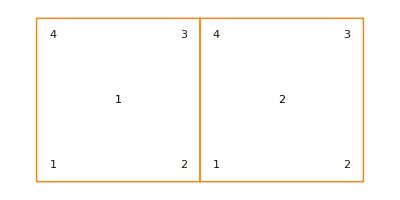

```mathematica
Module[{tiling},
tiling={
{{TestTile,4}},
{{TestTile,4},{1,0}}
};
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True]]/.TilingStyle[]
]
```

EmbedTiling[tiling, decorations, opts] takes a tilespec and a list decorations, and returns a list of the embeddings applied to each decoration, in turn.

This is typically used to overlay the Tiling decoration on top of a CreasePattern or FoldedForm2D decoration.

```mathematica
EmbedTiling[tiling_List,decorations_List,opts___]:=EmbedTiling[tiling,#,opts]&/@decorations
```

#### JoinTiling[tilespecs, opts] (options) Simplification, Numeric

JoinTiling[tilespecs] takes an ordered list of tilespecs and returns a modified list where all but the first tile are placed relative to earlier tiles in the list according to the offset specification for each tile. In the list, the offset, scale, and rotation for the first tile are left as specified, but for each subsequent tile, the offset for each tile is interpreted as an index list {i, j, ...} that determines the relative placement of that tile in the returned list of tilespecs. The {offset, rotation, scale} for the each depends on the format of the entries {i, j, ...}, as follows:
	{i, j, k} — the tile is offset so that the jth vertex of the ith tile is the position of the kth vertex of this tile AND rotate and scale the tile so that the (k–1)th vertex of the tile comes into alignment with the (j+1)th vertex of the ith tile, i.e., the edges mate.
	{i, j, –k} — the tile is offset so that the jth vertex of the ith tile is the position of the kth vertex of this tile, but leave rotation and scale as specified.
	{i, j, ±k, {x,y}} — Same thing as {i, j, ±k}, but add an additional offset {x,y} to the position. Good for making exploded tilings.

Options are:
	Simplification → Automatic | None, to Simplify the computed offset (and, if computed, scale and rotation) at each stage. This helps reduce the number of distinct tiletypes when embedding.
	Numeric → True | False. If True, make the computed {offset, rotation, scale} numeric. This can speed things up a lot if the TileVertices returned by RenderTile are symbolic and complex.

```mathematica
Options[JoinTiling]={
Simplification->Automatic,
Numeric->False
};
```

```mathematica
JoinTiling::badoffset="The offset `1` in tilespec `2` is improperly formatted for JoinTiling.";
```

```mathematica
JoinTiling[{}]:={};
```

```mathematica
JoinTiling[tilespecs_List,opts___]:=Module[{si,nm,sfn,out,tverts,tilespec,tiletype,offset,rotation,scale,verts,i,j,k,aoffset},
si=Simplification/.{opts}/.Options[JoinTiling];
nm=Numeric/.{opts}/.Options[JoinTiling];
sfn=If[si===Automatic,If[nm,N,#&],Simplify];
out={tilespecs⟦1⟧};
tverts={EmbedTile[tilespecs⟦1⟧,TileVertices,opts]};
Do[
tilespec=tilespecs⟦n⟧;
tiletype=tilespec⟦1⟧;
offset=If[Length[tilespec]≥2,tilespec⟦2⟧,{0,0}];
rotation=If[Length[tilespec]≥3,tilespec⟦3⟧,0];
scale=If[Length[tilespec]≥4,tilespec⟦4⟧,1];
verts=EmbedTile[{tiletype,{0,0},rotation,scale},TileVertices,opts];
aoffset={0,0};
Switch[Length[tilespec⟦2⟧],
3,{i,j,k}=tilespec⟦2⟧,
4,{i,j,k,aoffset}=tilespec⟦2⟧,
_,Message[JoinTiling::badoffset,tilespec⟦2⟧,tilespec];Abort[]];
If[k<0,
offset=sfn[tverts⟦i,j⟧-verts⟦Abs[k]⟧]+aoffset,
(* k>0 *)
{scale,rotation,offset}=ScaleRotationOffset[{verts⟦k⟧,verts⟦Mod[k-1,Length[verts],1]⟧},{tverts⟦i,j⟧,tverts⟦i,Mod[j+1,Length[tverts⟦i⟧],1]⟧}];
offset+=aoffset];
AppendTo[out,{tiletype,sfn[offset],sfn[rotation],sfn[scale]}];
AppendTo[tverts,sfn[EmbedTile[out⟦-1⟧,TileVertices,opts]]]
,{n,2,Length[tilespecs]}];
out]
```

Example: align vertex 5 of tile 2 to vertex 3 of tile 1 but leave rotation and scale unchanged.

```mathematica
Module[{tilespecs,tilespecs1},
tilespecs={
{{TestTile,4},{0,0}},
{{TestTile,5},{1,3,-5}}};
tilespecs1=JoinTiling[tilespecs,Numeric->True];
PrintThis[tilespecs1];
Graphics[EmbedTiling[tilespecs1,Tiling,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

Example: align vertex 1 of tile 2 to vertex 2 of tile 1 and vertex 5 of tile 2 to vertex 3 of tile 1 so that the edges line up.

```mathematica
Module[{tilespecs,tilespecs1},
tilespecs={
{{TestTile,4},{0,0}},
{{TestTile,5},{1,2,1}}};
tilespecs1=JoinTiling[tilespecs,Numeric->True];
Graphics[EmbedTiling[tilespecs1,Tiling,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

Example: align vertex 1 of tile 2 to vertex 2 of tile 1 and vertex 5 of tile 2 to vertex 3 of tile 1 so that the edges line up, but then throw in an additional offset between them. Also compare timing with and without the Numeric option. (Big difference.)

```mathematica
Module[{tilespecs,tilespecs1,t1,t2},
tilespecs={
{{TestTile,4},{0,0}},
{{TestTile,5},{1,2,1,{0.1,0}}}};
t1=Timing[tilespecs1=JoinTiling[tilespecs,Numeric->False]];
t2=Timing[tilespecs1=JoinTiling[tilespecs,Numeric->True]];
Print["Timing (Numeric→False) = ",t1⟦1⟧];
Print["Timing (Numeric→True) = ",t2⟦1⟧];
Graphics[EmbedTiling[tilespecs1,Tiling,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

Example: connect a triangle, square, triangle.

```mathematica
Module[{tilespecs,tilespecs1},
tilespecs={
{{TestTile,3},{0,0}},
{{TestTile,4},{1,2,1}},
{{TestTile,3},{2,2,1}}
};
tilespecs1=JoinTiling[tilespecs];
Graphics[EmbedTiling[tilespecs1,Tiling,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

### Pruned tilings

#### Notes

These functions are used for pruning tilings to the minimum necessary to cover convex polygonal regions. Some tiling generation functions, such as the Archimedean lattice tilings that we will encounter below, naturally generate very irregular-shaped regions of tiles (as always, defined by lists of tilespecs). Using these functions, we can prune a larger (possibly irregular) tiling down to a roughly rectangular tiling prior to rendering. This keeps the rendering time low, and if we export a tiling with a clipping rectangle, this ensures that unnecessary tiles outside of the cliprect are not rendered.

#### TilespecInPolygonQ[tilespec, verts]

TilespecInPolygonQ[tilespec, verts] takes a tilespec and returns true if any part of the tile lies within the specified convex polygon verts. It does this by looking at whether any of the vertices of the tile lie within the polygon or vice-versa. It relies on convexity of both polygons.

TBD: this will fail if we have two crossed rectangles that overlap without enclosing each others vertices. In Mathematica 10, there are nice built-in functions for determining polygon intersection, so we’ll use those at the next upgrade.

```mathematica
TilespecInTilingQ[tilespec_,verts_]:=Module[{pts},
pts=EmbedTile[tilespec,TileVertices,Numeric->True];
Or@@Join[PtInConvexPolygonQ[#,verts]&/@pts,PtInConvexPolygonQ[#,pts]&/@verts ]]
```

Examples.

```mathematica
Module[{tilespec,cliprect},
tilespec={{TestTile,4},{1.1,0},10°};
cliprect=SquareVertices[1.];
Print[Graphics[{
EmbedTiling[{tilespec},Tiling],Style[Line[Append[cliprect,cliprect⟦1⟧]],
AbsoluteThickness[2],Red]}]/.TilingStyle[]];
TilespecInTilingQ[tilespec,cliprect]
]//ShowExample
```

```mathematica
Module[{tilespec,cliprect},
tilespec={{TestTile,4},{1.3,0},10°};
cliprect=SquareVertices[1.];
Print[Graphics[{
EmbedTiling[{tilespec},Tiling],Style[Line[Append[cliprect,cliprect⟦1⟧]],
AbsoluteThickness[2],Red]}]/.TilingStyle[]];
TilespecInTilingQ[tilespec,cliprect]
]//ShowExample
```

#### PruneTiling[tilespecs, verts]

PruneTiling[tilespecs, verts] takes the tiling specified by tilespecs and eliminates any tiles that lie wholly outside of the convex polygon verts, returning the reduced list of tilespecs. The clipping polygon verts is given as a list of coordinate pairs for the vertices of the clipping polygon.

```mathematica
PruneTiling[tilespecs_,verts_List]:=Select[tilespecs,TilespecInTilingQ[#,verts]&]
```

Example: compare without pruning and with pruning. Red outlines the pruning polygon.

```mathematica
Module[{tilespecs,cliprect,ptilespecs},
tilespecs=Flatten[Table[{{TestTile,4},{-.1+i-1,-.1+j-1}},{i,4},{j,4}],1];
cliprect=SquareVertices[2.3];
ptilespecs=PruneTiling[tilespecs,cliprect];
GraphicsRow[{
Graphics[{
EmbedTiling[tilespecs,Tiling],
Style[Line[Append[cliprect,cliprect⟦1⟧]],AbsoluteThickness[2],Red]},PlotLabel->"unpruned"],
Graphics[{
EmbedTiling[ptilespecs,Tiling],
Style[Line[Append[cliprect,cliprect⟦1⟧]],AbsoluteThickness[2],Red]},PlotLabel->"pruned"]}/.TilingStyle[]]
]//ShowExample
```

#### PrunePoly[verts]

PrunePoly[verts] returns Graphics elements of a red-outlined polygon of verts. Provided as a convenience because we often want to show this when we’re pruning lists of tilespecs.

```mathematica
PrunePoly[verts_List]:=Style[Line[Append[verts,verts⟦1⟧]],AbsoluteThickness[2],Red]
```

### Crease-assigned graph decorations

#### Notes

The tiling infrastructure is not inherently tied to origami; it can be used to create and manipulate tilings purely as decorative patterns. But the main reason we went to the trouble of creating the infrastructure is to easily generate crease patterns and folded forms of origami tessellations, when described as tilings of smaller building blocks.

Usually, for an origami tessellation, we are interested in both crease pattern and folded form, and for many types of tessellation, the tiles for crease pattern and for folded form are geometrically similar to one another, meaning the folded form has the same vertices, just smaller. For those patterns, we can create both CP and FF renderings using the tiling infrastructure by creating a CreasePattern decoration of the relevant tiles and a FoldedForm2D or FoldedForm3D decoration of the relevant tiles, and then use the tiling infrastructure to combine those decorations with a particular tiling.

Although it is certainly possible to create CreasePattern and FoldedForm2D or FoldedForm3D renderings directly, for most tiles, the way we will create the crease pattern and folded form tiles is to create a TGraphAssigned, TGraph2DAssigned, or TGraph3DAssigned, and then construct the crease pattern and folded form elements by rendering those using the standard rendering functions. So, we introduce those three forms as possible decorations.

There is an important limitation on using the tiling infrastructure to render the folded forms, though: since we are essentially placing CP tiles and FF tiles on the same underlying tiling, this will only work if the folded form of a CP tile has TileVertices that are geometrically similar to those of the CP tile, so that we can create a FF tile that is a geometrically scaled version of the actual FF that can be placed on the same tiling.

For 3D tilings, we assume the tiling lies in the x-y plane.

#### Tiling decorations TGraphAssigned, TGraph2DAssigned, TGraph3DAssigned

A TGraphAssigned, TGraph2DAssigned, or TGraph3DAssigned is a type of decoration of a tiling. Embedding a tiling with one of these decorations will return a list of that type of TObj class placed according to the size, position, and orientation specified in the tiling.

We will also use the embedding of a single tile with one of these decorations as an intermediate step in rendering crease pattern and/or folded form decorations.

#### EmbedTile[{tiletype, offset, rotation, scale}, TGraphAssigned, opts] (options) Numeric

EmbedTile[{tiletype, offset, rotation, scale}, TGraph, opts] embeds a tile as a TGraph with the specified placement.

```mathematica
EmbedTile[{tiletype_List,offset_:{0,0},rotation_:0,scale_:1},TGraphAssigned,opts___]:=Module[{nm,dtile,verts},
nm=Numeric/.{opts}/.Options[EmbedTile];
dtile=RenderTileCache[tiletype,TGraphAssigned,opts];
verts=If[nm,N[offset+RotationMatrix2D[rotation].(scale*#)]&,(offset+RotationMatrix2D[rotation].(scale*#))&]/@dtile[Vertices];
dtile//ReplaceProperty[Vertices->verts]]
```

#### EmbedTile[{tiletype, offset, rotation, scale}, TGraph2DAssigned, opts] (options) Numeric

EmbedTile[{tiletype, offset, rotation, scale}, TGraph2D, opts] embeds a tile as a TGraph2DAssigned with the specified placement.

```mathematica
EmbedTile[{tiletype_List,offset_:{0,0},rotation_:0,scale_:1},TGraph2DAssigned,opts___]:=Module[{nm,dtile,verts,verts2d,f2d},
nm=Numeric/.{opts}/.Options[EmbedTile];
dtile=RenderTileCache[tiletype,TGraph2DAssigned,opts];
f2d=If[nm,N[offset+RotationMatrix2D[rotation].(scale*#)]&,(offset+RotationMatrix2D[rotation].(scale*#))&];
verts=f2d/@dtile[Vertices];
verts2d=f2d/@dtile[Vertices2D];
dtile//ReplaceProperties[{Vertices->verts,Vertices2D->verts2d}]]
```

#### EmbedTile[{tiletype, offset, rotation, scale}, TGraph3DAssigned, opts] (options) Numeric

EmbedTile[{tiletype, offset, rotation, scale}, TGraph3D, opts] embeds a tile as a TGraph3DAssigned with the specified placement.

```mathematica
EmbedTile[{tiletype_List,offset_:{0,0},rotation_:0,scale_:1},TGraph3DAssigned,opts___]:=Module[{nm,dtile,verts,verts3d,f2d,f3d},
nm=Numeric/.{opts}/.Options[EmbedTile];
dtile=RenderTileCache[tiletype,TGraph3DAssigned,opts];
f2d=If[nm,N[offset+RotationMatrix2D[rotation].(scale*#)]&,(offset+RotationMatrix2D[rotation].(scale*#))&];
f3d=If[nm,N[Append[offset,0]+RotationZMatrix3D[rotation].(scale*#)]&,(Append[offset,0]+RotationZMatrix3D[rotation].(scale*#))&];
verts=f2d/@dtile[Vertices];
verts3d=f2d/@dtile[Vertices3D];
dtile//ReplaceProperties[{Vertices->verts,Vertices3D->verts3d}]]
```

### Crease patterns and folded form decorations

#### Tiling decorations CreasePattern, FoldedForm2D, FoldedForm3D

CreasePattern, FoldedForm2D, and FoldedForm3D are decorations that produce renditions of the crease pattern and folded form for a tile.

```mathematica
CreasePattern::usage="CreasePattern is a type of tile decoration that displays a crease pattern tile.";
```

```mathematica
FoldedForm2D::usage="FoldedForm2D is a type of tile decoration that displays a flat folded form tile.";
```

```mathematica
FoldedForm3D::usage="FoldedForm3D is a type of tile decoration that displays a 3D folded form tile.";
```

#### RenderTile[tiletype, CreasePattern, opts] RenderTile[tiletype, FoldedForm2D, opts] RenderTile[tiletype, FoldedForm3D, opts]

RenderTile[tiletype, CreasePattern, opts] constructs the CreasePattern tile from the TGraphAssigned tile but renders without border lines.

```mathematica
RenderTile[tiletype_List,CreasePattern,opts___]:=Module[{tobj},
tobj=RenderTile[tiletype,TGraphAssigned,opts];
CreasePatternGraphics[tobj]⟦1⟧//KillBorder]
```

RenderTile[tiletype, FoldedForm2D, opts] constructs the FoldedForm2D tile from the TGraph2DAssigned tile but renders without border lines.

```mathematica
RenderTile[tiletype_List,FoldedForm2D,opts___]:=Module[{tobj},
tobj=RenderTile[tiletype,TGraph2DAssigned,opts];
VisibleFoldedFormGraphics[tobj]⟦1⟧//KillBorder]
```

RenderTile[tiletype, FoldedForm3D, opts] constructs the FoldedForm3D tile from the TGraph3DAssigned tile but renders without border lines.

```mathematica
RenderTile[tiletype_List,FoldedForm3D,opts___]:=Module[{tobj},
tobj=RenderTile[tiletype,TGraph3DAssigned,opts];
FoldedFormGraphics3D[tobj]⟦1⟧//KillBorder]
```

Examples are given below for specific tiletypes.

### Tiling arrows

#### Notes

Here we define four different styles for drawing edge arrows on tilings. Arrows could be Directed (D, along the edge) or Crossing (C, transverse to the edge), and Half (H) or Full (F).

#### TileArrowDH[{p, q}, dir] TileArrowCH[{p, q}, dir] TileArrowDF[{p, q}, dir] TileArrowCF[{p, q}, dir]

TileArrowDH[{p, q}, dir] returns a directed half-arrowhead on the CCW side of the line from p to q. If dir>0, then p is the tail; otherwise q is the tail.

```mathematica
TileArrowDH[{p_,q_}, dir_]:=Module[{r,s,ctr,sz,w,pts},
r=q-p;
s=Rotate90[r];
ctr=(p+q)/2;
sz=0.15;
w=0.58;
pts=ctr+sz#&/@ If[dir>0,
{-.5 r,+.5 r,-.5 r+w s},
{+.5 r,-.5 r,+.5 r+w s}];
Style[Polygon[pts],TilingLine]]
```

Example

```mathematica
Module[{pts1,pts2},
pts1={{0,0},{1,0}};
pts2={{1,0},{1,0.7}};
Graphics[{
{Line[pts1],TileArrowDH[pts1,+1]},
{Line[pts2],TileArrowDH[pts2,-1]}}]/.TilingStyle[]
]//ShowExample
```

TileArrowCH[{p, q}, dir] returns a crossing arrowhead entirely on the CCW side of the line from p to q. If dir>0, then the arrow points to the right (relative to the line from p to q); otherwise it points to the left.

```mathematica
TileArrowCH[{p_,q_}, dir_]:=Module[{r,s,ctr,sz,w,pts},
r=q-p;
s=Rotate90[r];
ctr=(p+q)/2;
sz=0.15;
w = 0.3;
pts=ctr+sz#&/@If[dir>0,
{{0,0},s+w r,s-w r},
{-w r,w r,s}];
Style[Polygon[pts],TilingLine]]
```

Example

```mathematica
Module[{pts1,pts2},
pts1={{0,0},{1,0}};
pts2={{1,0},{1,0.7}};
Graphics[{
{Line[pts1],TileArrowCH[pts1,+1]},
{Line[pts2],TileArrowCH[pts2,-1]}}]/.TilingStyle[]
]//ShowExample
```

TileArrowDF[{p, q}, dir] returns a directed full arrowhead centered on the line from p to q. If dir>0, then p is the tail; otherwise q is the tail.

```mathematica
TileArrowDF[{p_,q_}, dir_]:=Module[{r,s,ctr,sz,w,pts},
r=q-p;
s=Rotate90[r];
ctr=(p+q)/2;
sz=0.18;
w=0.3;
pts=ctr+sz#&/@ If[dir>0,
{-.5 r-w s,+.5 r,-.5 r+w s},
{+.5 r-w s,-.5 r,+.5 r+w s}];
Style[Polygon[pts],TilingLine]]
```

Example

```mathematica
Module[{pts1,pts2},
pts1={{0,0},{1,0}};
pts2={{1,0},{1,0.7}};
Graphics[{
{Line[pts1],TileArrowDF[pts1,+1]},
{Line[pts2],TileArrowDF[pts2,-1]}}]/.TilingStyle[]
]//ShowExample
```

TileArrowCF[{p, q}, dir] returns a crossing arrowhead centered on the line from p to q. If dir>0, then the arrow points to the right (relative to the line from p to q); otherwise it points to the left.

```mathematica
TileArrowCF[{p_,q_}, dir_]:=Module[{r,s,ctr,sz,w,pts},
r=q-p;
s=Rotate90[r];
ctr=(p+q)/2;
sz=0.18;
w=0.3;
pts=ctr+sz#&/@If[dir>0,
{-.5s,.5s+w r,.5s-w r},
{-w r-.5s,w r-.5s,.5s}];
Style[Polygon[pts],TilingLine]]
```

Example

```mathematica
Module[{pts1,pts2},
pts1={{0,0},{1,0}};
pts2={{1,0},{1,0.7}};
Graphics[{
{Line[pts1],TileArrowCF[pts1,+1]},
{Line[pts2],TileArrowCF[pts2,-1]}}]/.TilingStyle[]
]//ShowExample
```

### Polygon tiles

#### Notes

For a general polygonal tile, the tile is described as an ordered list of its vertices. By convention, the vertices of a tile should rotate counterclockwise. We start by defining some standard rendering conventions for tilings.

We set up a general-purpose tile, PolygonTile, with lots of options that we can use as a general tool for representing outlined tilings. Most other specialized tiles will use RenderTile[{PolygonTile,...] as their rendering function for the decorations TileVertices and Tiling, while then creating more specialized implementations for other decorations.

#### {PolygonTile, verts}

```mathematica
PolygonTile::usage="PolygonTile is a tile type that specifies a polygon by its vertices.";
```

#### RenderTile[{PolygonTile, verts}, TileVertices, opts] RenderTile[{PolygonTile, verts}, Tiling, opts] (options) TilePolys, TileEdges, TileVertexIndices, TileEdgeArrowStyle, TilePolyFill, TileEdgeArrowDirs, TileIndex

RenderTile[{PolygonTile, verts}, TileVertices, opts] returns verts as the vertices of the tile.

```mathematica
RenderTile[{PolygonTile,verts_List},TileVertices,opts___]:=verts
```

Example

```mathematica
RenderTile[{PolygonTile,UnitRegularPolygonVertices[4]},TileVertices]
```

{{0,0},{1,0},{1,1},{0,1}}

RenderTile[{PolygonTile, verts}, Tiling, opts] returns a list of Graphics elements that render a tile with vertices verts. Options are:
	(global options)
	TilePolys → True | False, specifies whether to render tile polygon with a fill pattern.
	TileEdges → True | False, specifies whether to render te edges of the tile polygon.
	TileVertexIndices → True | False, specifies whether to draw vertex indices in the corners of the polygon. 
	TileEdgeArrowStyle → TileArrowDH | TileArrowCH | TileArrowDF | TileArrowCF | None, specifies the style for rendering an edge type (M or V). This option has no effect if EdgeTypes is not provided.
	( tile-specific options)
	TilePolyFill → M | V | W | O | None, specifies what fill color to use for the polygon of the tile.
	TileEdgeArrowDirs → list | None, where list, if provided, has entries M or V, one for each edge of the tile.
	TileIndex → label | None, specifies whether to draw  label in the center of the polygon.

There are two types of options: those that turn on/off rendering typically for an entire tiling, and those that are used to alter individual tiles in different ways. TileIndex, TilePolyFill and TileEdgeArrowDirs are in the latter category; these options will typically be set by more specialized RenderTile implementations that are built upon the PolygonTile type. Note that TileIndex may be passed in from EmbedTiling.

```mathematica
TilePolys::usage="TilePolys is an option to RenderTile[{PolygonTile, verts}, Tiling, opts] that specifies whether to render tile polygons with a fill color.";
```

```mathematica
TileEdges::usage="TileEdges is an option to RenderTile[{PolygonTile, verts}, Tiling, opts] that specifies whether to render the edges of time polygons.";
```

```mathematica
TileVertexIndices::usage="TileVertexIndices is an option to RenderTile[{PolygonTile, verts}, Tiling, opts] that specifies whether to label the indices of the vertices of the tile.";
```

```mathematica
TileEdgeArrowStyle::usage="TileEdgeArrowStyle is an option to RenderTile[{PolygonTile, verts}, Tiling, opts] that specifies the arrowhead style to use on the edges of the tile.";
```

```mathematica
TilePolyFill::usage="TilePolyFill is an option to RenderTile[{PolygonTile, verts}, Tiling] that specifies the symbolic fill color to use for the tile.";
```

```mathematica
TileEdgeArrowDirs::usage="TileEdgeArrowDirs is an option to RenderTile[{PolygonTile, verts}, Tiling, opts] that specifies a list of directions (±1) for each edge of the tile.";
```

Note that the default options only draw the outline of the tile. For everything else, you must turn on the option explicitly.

```mathematica
Options[PolygonTile]={
TilePolys->False,
TileEdges->True,
TileVertexIndices->False,
TileEdgeArrowStyle->None,
TilePolyFill->None,
TileEdgeArrowDirs->None,
TileIndex->None
};
```

```mathematica
PolygonTile::badpolys="Value `1` to option TilePolys should be True or False.";
```

```mathematica
PolygonTile::badedges="Value `1` to option TileEdges should be True or False.";
```

```mathematica
PolygonTile::badvertinds="Value `1` to option TileVertexIndices should be True or False.";
```

```mathematica
PolygonTile::badpolytype="`1` is an invalid specification for TilePolyFill.";
```

```mathematica
PolygonTile::badedgetypes = "The length `1` of EdgeTypes `2` does not match the length `3` of vertices `4`.";
```

```mathematica
PolygonTile::badedgearrows="`1` is an invalid specification for TileEdgeArrowStyle.";
```

```mathematica
RenderTile[{PolygonTile,verts_List},Tiling,opts___]:=Module[{tp,te,pt,et,ea,ci,vi,n,ctr,out,fill,edges},
tp=TilePolys/.{opts}/.Options[PolygonTile];
te=TileEdges/.{opts}/.Options[PolygonTile];
vi=TileVertexIndices/.{opts}/.Options[PolygonTile];
ea=TileEdgeArrowStyle/.{opts}/.Options[PolygonTile];
pt=TilePolyFill/.{opts}/.Options[PolygonTile];
et=TileEdgeArrowDirs/.{opts}/.Options[PolygonTile];
ci=TileIndex/.{opts}/.Options[PolygonTile];
n=Length[verts];
ctr=(Plus@@verts)/n;
edges=Transpose[{verts,RotateLeft[verts]}];
out={};
(* fill *)
Switch[tp,
True,If[!(pt===None),AppendTo[out,Style[Polygon[verts],pt]]],
False,Null,
_,Message[PolygonTile::badpolys,tp];Abort[]];
(* lines *)
Switch[te,
True,AppendTo[out,Style[Line[#],TilingLine]&/@edges],
False,Null,
_,Message[PolygonTile::badedges,te];Abort[]];
(* arrowheads *)
If[!(ea===None||et===None),
If[Length[et]≠Length[verts],Message[PolygonTile::badedgetypes,Length[et],et,Length[verts],verts];Abort[]];
If[Position[{TileArrowDH,TileArrowCH,TileArrowDF,TileArrowCF},ea]=={},Message[PolygonTile::badedgearrows,ea];Abort[]];
AppendTo[out,MapThread[ea,{edges,et}]]];
(* tiling index *)
If[!(ci===None),AppendTo[out,Style[Text[ToString[ci],ctr],TilingText]]];
(* vertex indices *)
Switch[vi,
True,AppendTo[out,Style[Table[Text[ToString[j],0.8 verts⟦j⟧+0.2ctr],{j,n}],TilingText]],
False,Null,
_,Message[PolygonTile::badvertinds,vi];Abort[]];
out]
```

Examples. Different fills.

```mathematica
Module[{verts},
verts=UnitRegularPolygonVertices[4];
GraphicsRow[{
Graphics[RenderTile[{PolygonTile,verts},Tiling],PlotLabel->"none"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TilePolys->True,TilePolyFill->TilingNoFill],PlotLabel->"TilingNoFill"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TilePolys->True,TilePolyFill->TilingLightFill],PlotLabel->"TilingLightFill"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TilePolys->True,TilePolyFill->TilingMedFill],PlotLabel->"TilingMedFill"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TilePolys->True,TilePolyFill->TilingDarkFill],PlotLabel->"TilingDarkFill"]
}]/.TilingStyle[]
]//ShowExample
```

Example. Different edge arrows.

```mathematica
Module[{verts},
verts=UnitRegularPolygonVertices[4];
GraphicsRow[{
Graphics[RenderTile[{PolygonTile,verts},Tiling,TileEdgeArrowDirs->{1,1,-1,-1}],PlotLabel->"none"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TileEdgeArrowDirs->{1,1,-1,-1},TileEdgeArrowStyle->TileArrowDH],PlotLabel->"TileArrowDH"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TileEdgeArrowDirs->{1,1,-1,-1},TileEdgeArrowStyle->TileArrowCH],PlotLabel->"TileArrowCH"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TileEdgeArrowDirs->{1,1,-1,-1},TileEdgeArrowStyle->TileArrowDF],PlotLabel->"TileArrowDF"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TileEdgeArrowDirs->{1,1,-1,-1},TileEdgeArrowStyle->TileArrowCF],PlotLabel->"TileArrowCF"]
}]/.TilingStyle[]
]//ShowExample
```

Example. Stuff in the center and indexed vertices.

```mathematica
Module[{verts},
verts=UnitRegularPolygonVertices[4];
GraphicsRow[{
Graphics[RenderTile[{PolygonTile,verts},Tiling],PlotLabel->"none"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TileIndex->"a"],PlotLabel->"TileIndex"],
Graphics[RenderTile[{PolygonTile,verts},Tiling,TileVertexIndices->True],PlotLabel->"TileVertexIndices"]
}]/.TilingStyle[]
]//ShowExample
```

## Twist tiles

#### Notes

Twist tiles are tiles that incorporate polygonal twists within a polygonal tile.

In general, the naming of a twist tile will follow this scheme: <shape>[<twisttype>]Tile, where
	<shape> describes the shape (outline) of the tile,
	<twisttype> (optional) describes the type of twist that is within the tile. 
So, for example, in UnitTrapezoidOffsetTwistTile, <shape> is UnitTrapezoid, <twisttype> is OffsetTwist.

### Polygon twist tiles

#### Notes

There is a general family of twist tiles that involves sending pleats in from the tile edges at a specified angle relative to the tile edge. The pleats intersect to create a central polygon. Two cases of particular interest are edge-centered twist tiles (PolygonCenteredTwistTile, PolygonCenteredTwistAlt) and offset twist tiles (PolygonOffsetTwistTile). We can implement both of these as special cases of a general-purpose tile, PolygonTwistTile, which we construct here.

You will normally not build tilings directly from this type of tile. We use it as a building block for other types of twist tiles. Note, too, that it is, in general, only flat-foldable for certain polygons and combinations of parameters.

#### {PolygonTwistTile, verts, w, d, τ, ccw, types}

{PolygonTwistTile, verts, w, d, τ, ccw, types} is a tiletype that describes a twist in a polygon specified by its vertices verts where w is the fractional width of each pleat where it subtends its edge, τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, d is the offset from the center of the edge, ccw is a flag indicating whether the pleat crease assignment should assume a CCW twist, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
PolygonTwistTile::usage="PolygonTwistTile is a tile type that produces a simple flat twist in a polygon.";
```

#### TileCheckTypes[verts, types]

TileCheckTypes[verts, types] checks the length of verts against the length of types and throws an error if there is a mismatch.

```mathematica
TileCheckTypes::badtypes="Length `1` of vertex list `2` does not match length `3` of types list `4`.";
```

```mathematica
TileCheckTypes[verts_List,types_List]:=If[Length[verts]≠Length[types],Message[TileCheckTypes::badtypes,Length[verts],verts,Length[types],types];Abort[]]
```

#### RenderTile[{PolygonTwistTile, verts, w, d, τ, ccw, types}, TileVertices, opts] RenderTile[{PolygonTwistTile, verts, w, d, τ, ccw, types}, Tiling, opts]

RenderTile[{PolygonTwistTile, verts, w, d, τ, ccw, types}, TileVertices, opts] returns the vertices of the tiling polygon.

```mathematica
RenderTile[{PolygonTwistTile,verts_List,w_,d_,τ_,ccw_,types_List},TileVertices,opts___]:=verts
```

Example.

```mathematica
Module[{verts,w,d,τ,ccw,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=0.1;
τ=70°;
ccw=True;
types={M,M,V,V};
RenderTile[{PolygonTwistTile,verts,w,d,τ,ccw,types},TileVertices]
]//ShowExample
```

RenderTile[{PolygonTwistTile, verts, w, d, τ, ccw, types}, Tiling, opts] returns a rendering of the tiling polygon with no additional decoration.

```mathematica
RenderTile[{PolygonTwistTile,verts_List,w_,d_,τ_,ccw_,types_List},Tiling,opts___]:=RenderTile[{PolygonTile,verts},Tiling,opts]
```

Example.

```mathematica
Module[{verts,w,d,τ,ccw,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=0.1;
τ=70°;
ccw=True;
types={M,M,V,V};
Graphics[RenderTile[{PolygonTwistTile,verts,w,d,τ,ccw,types},Tiling]]/.TilingStyle[]
]//ShowExample
```

#### CP/FF equivalence

In this section we generate TGraphAssigned and TGraph2DAssigned tiles for the crease pattern and (ostensible) folded form tile of general simple flat twist tiles. If the crease pattern is flat-foldable (not necessarily the case for all parameters), then the folded form tile is geometrically similar to a crease pattern tile with different {w, d, τ} parameters, and we can use that fact to compute an equivalent tile for the folded form.

Here we compute equivalent {w’, d’, τ’} parameters for a folded form tile. Line OABP is the original tile edge. Line OACP’ is the folded image of the edge. Line OP’ is the folded form tile edge; distances and angles are computed relative to it.

```mathematica
Module[{O,A,B,C,P,Pp,Ap,Bp,τp,soln,ex},
O={0,0};
A={(1-w)/2+d,0};
B={(1+w)/2+d,0};
P={1,0};
C=B+2 w Sin[τ] {-Sin[τ],Cos[τ]};
Pp=P+2 w Sin[τ] {-Sin[τ],Cos[τ]};
Ap=LineInt2D[O,Pp-O,A,U[τ]];
Bp=LineInt2D[O,Pp-O,C,U[τ]];
(* equivalent tilt angle for folded form *)
τp=FullSimplify[ArcTan[(U[τ-π/2].(Pp-O))/(U[τ].(Pp-O))]];
Print["τ' = ",τp];
soln=FullSimplify[Solve[{(1-wp)/2+dp==((Ap-O)⟦1⟧)/((Pp-O)⟦1⟧),(1+wp)/2+dp==((Bp-O)⟦1⟧)/((Pp-O)⟦1⟧)},{wp,dp}]];
Print["w' = ",wp/.soln⟦1⟧,", d' = ",dp/.soln⟦1⟧];
(* and show a plot of the geometry *)
ex={w->0.15,d->-0.08,τ->70°};
Graphics[{
Black,Line[{O,P}],
Gray,Line[{A,A+.5U[τ]}],Line[{B,B+.5U[τ]}],Line[{C,C+.5U[τ]}],
Orange,Line[{O,Pp}],
Green,Line[{A,C,Pp}],
LightGray,Line[{B,C}],Line[{P,Pp}],Line[{C-.1U[τ],C}],
Black,
Point[O],Text["O",O,{2,0}],
Point[A],Text["A",A,{0,2}],
Point[B],Text["B",B,{0,2}],
Point[C],Text["C",C,{0,-2}],
Point[P],Text["P",P,{-2,0}],
Point[Pp],Text["P'",Pp,{-2,0}],
Point[Ap],Text["A'",Ap,{0,-2}],
Point[Bp],Text["B'",Bp,{1,-2}],
{}}]/.ex
]//ShowExample
```

#### RenderTile[{PolygonTwistTile, verts, w, d, τ, ccw, types}, TGraphAssigned, opts]

RenderTile[{PolygonTwistTile, verts, w, d, τ, ccw, types}, TGraphAssigned, opts] returns a TGraphAssigned+TTwistGraph that describes the creases for a twist in polygon specified by its vertices verts where w is the fractional width of each pleat where it subtends its edge, τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, d is the offset from the center of the edge, ccw is a flag indicating whether the pleat crease assignment should assume a CCW twist, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{PolygonTwistTile,verts_List, w_,d_, τ_,ccw_,types_List},TGraphAssigned,opts___] := Module[{n,gverts,dirs,cverts,averts,edges,atypes,twistface,faces,pleats,wedges},
TileCheckTypes[verts,types];
n=Length[verts];
(* vertices on tile boundary *)
gverts=MapThread[{#1,(1+w)/2#1+(1-w)/2#2+d(#2-#1),(1-w)/2#1+(1+w)/2#2+d(#2-#1)}&,{verts,RotateLeft[verts]}];
dirs=RotationMatrix2D[τ].#&/@(RotateLeft[verts]-verts);
(* central polygon vertices *)
cverts=MapThread[LineInt2D,{#⟦2⟧&/@gverts,dirs,#⟦3⟧&/@RotateRight[gverts],RotateRight[dirs]}];(* all vertices *)
averts=Flatten[MapThread[Append,{gverts,cverts}],1];
edges=Mod[Flatten[Table[{{1,2},{2,3},{3,5},{2,4},{3,8},{4,8}}+4i,{i,0,n-1}],1],4n,1];
atypes=Flatten[{B,B,B,If[ccw,#,InvertFoldType[#]],If[ccw,InvertFoldType[#],#],#}&/@types];
pleats=Mod[Table[{2,3,8,4}+4i,{i,0,n-1}],4n,1];
wedges=Mod[Table[{1,2,4,-1}+4i,{i,0,n-1}],4n,1];
twistface=Mod[Table[4i,{i,n}],4n,1];
faces=Join[{twistface},pleats,wedges];
MakeTGraph[averts,edges,faces]//AddTAssigned[atypes]//AddTTwistGraph[{1}]]
```

Example. A centered twist tile.

```mathematica
Module[{verts,w,d,τ,ccw,types,tobj},
verts={{0,0},{1,0},{1/2,1}};
w=0.15;
d=0;
τ=75°;
ccw=True;
types={M,M,M};
tobj=RenderTile[{PolygonTwistTile,verts,w,d,τ ,ccw,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

Example. An offset twist tile.

```mathematica
Module[{verts,w,d,τ,ccw,types,tobj},
verts={{0,0},{1,0},{1/2,1}};
w=0.16;
d=0.08;
τ=90°;
ccw=True;
types={M,M,M};
tobj=RenderTile[{PolygonTwistTile,verts,w,d,τ ,ccw,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

#### RenderTile[{PolygonTwistTile, verts, w, d, τ, ccw, types}, TGraph2DAssigned, opts] (options) Tolerance

RenderTile[{PolygonTwistTile, verts, w, τ, types}, TGraph2DAssigned, opts] returns a TGraph2DAssigned+TTwistGraph for the folded form of a unit polygon twist. So it contains Vertices for the CP and Vertices2D for the FF, but note that they are at different relative scale, so as to fit within the same tile. That is, the FF is not actually what you’d get if you folded the CP, but rather, it is the geometrically similar folded form tile.

```mathematica
RenderTile[{PolygonTwistTile,verts_List, w_,d_, τ_,ccw_,types_List},TGraph2DAssigned,opts___] := Module[{tobjcp,tobjff},
tobjcp=RenderTile[{PolygonTwistTile,verts,w,d,τ,ccw,types},TGraphAssigned,opts];
tobjff=RenderTile[{PolygonTwistTile,verts,-w/(1-2w),d/(1-2 w),ArcCot[Cot[τ]/(1-2w)],ccw,types},TGraphAssigned,opts];
tobjcp//AddTGraph2D[tobjff[Vertices]]]
```

Example: TGraph2D tile. You can tell that the folded form polygon is at a different scale because the central polygon is larger.

```mathematica
Module[{verts,w,d,τ,ccw,types,tobj},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=-0.05;
τ=70°;
ccw=True;
types={M,M,V,V};
tobj=RenderTile[{PolygonTwistTile,verts,w,d,τ,ccw,types},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

### Polygon twist graph properties

#### Notes

For a general polygon twist, the twist crease pattern isn’t necessarily flat foldable, because the twist angles vary around the central polygon. We can use the functions in this section to probe geometric properties of such polygons.

#### PolygonTwistNumSides[tobj] (unchecked class) TGraphAssigned

PolygonTwistNumSides[tobj] takes a TGraphAssigned of a n-gon twist tile and returns the number of sides of the tile and central polygon. (Which we can get because the central polygon is always the first polygon in the face list.)

```mathematica
PolygonTwistNumSides[tobj_TObj]:=Length[tobj[Faces]⟦1⟧]
```

Example

```mathematica
Module[{verts,tobj},
verts={{0,0},{1,0},{.8,.9},{-.1,.7}};
tobj=RenderTile[{PolygonTwistTile,verts,.2,.2,90°,True,{M,M,V,V}},TGraphAssigned];
Print["Num sides = ",PolygonTwistNumSides[tobj]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### PolygonTwistTwistAngles[tobj] (unchecked class) TGraphAssigned

PolygonTwistTwistAngles[tobj] takes a TGraphAssigned of a polygon twist tile and returns a list of the twist angles at the central polygon.

```mathematica
PolygonTwistTwistAngles[tobj_TObj]:=Module[{n,v,p,q,r},
n=Length[tobj[Faces]⟦1⟧];
v=tobj[Vertices];
Table[
{p,q,r}=v⟦Mod[4i+{-1,4,0},Length[v],1]⟧;(* triples that define each twist angle *)
ArcTan[(p-q).(r-q),(p-q).(RotationMatrix2D[π/2].(r-q))],{i,n}]]
```

Example

```mathematica
Module[{verts,tobj},
verts={{0,0},{1,0},{.8,.9},{-.1,.7}};
tobj=RenderTile[{PolygonTwistTile,verts,.2,.2,90°,True,{M,M,V,V}},TGraphAssigned];
Print["Twist angles/° = ",PolygonTwistTwistAngles[tobj]/°];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### PolygonTwistCentralPolygonSides[tobj] (unchecked class) TGraphAssigned

PolygonTwistCentralPolygonSides[tobj] takes a TGraphAssigned of a polygon twist tile and returns a list of the side lengths of the central polygon.

```mathematica
PolygonTwistCentralPolygonSides[tobj_TObj]:=Module[{n,v,p,q},
n=Length[tobj[Faces]⟦1⟧];
v=tobj[Vertices];
Table[
{p,q}=v⟦Mod[4i+{0,4},Length[v],1]⟧;
Mag[p-q],{i,n}]]
```

Example

```mathematica
Module[{verts,tobj},
verts={{0,0},{1,0},{.8,.9},{-.1,.7}};
tobj=RenderTile[{PolygonTwistTile,verts,.2,.2,90°,True,{M,M,V,V}},TGraphAssigned];
Print["Central polygon side lengths = ",PolygonTwistCentralPolygonSides[tobj]];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### PolygonTwistCentralPolygonAngles[tobj] (unchecked class) TGraph

PolygonTwistCentralPolygonAngles[tobj] takes a TGraphAssigned of a polygon twist tile and returns a list of the corner angles of the central polygon.

```mathematica
PolygonTwistCentralPolygonAngles[tobj_TObj]:=Module[{n,v,p,q,r},
n=Length[tobj[Faces]⟦1⟧];
v=tobj[Vertices];
Table[
{p,q,r}=v⟦Mod[4i+{-4,0,4},Length[v],1]⟧;
π-ArcTan[(r-q).(q-p),(r-q).(RotationMatrix2D[π/2].(q-p))],{i,n}]]
```

Example

```mathematica
Module[{verts,tobj},
verts={{0,0},{1,0},{.8,.9},{-.1,.7}};
tobj=RenderTile[{PolygonTwistTile,verts,.2,.2,90°,True,{M,M,V,V}},TGraphAssigned];
Print["Central polygon corner angles/° = ",PolygonTwistCentralPolygonAngles[tobj]/°];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### PolygonTwistCentralPolygonAnglesExcess[tobj]

PolygonTwistCentralPolygonAnglesExcess[tobj] takes a TGraphAssigned of a polygon twist tile and returns a list of the Kawasaki excess at each of the corner angles of the central polygon.

```mathematica
PolygonTwistCentralPolygonAnglesExcess[tobj_TObj]:=Module[{ta},
ta=PolygonTwistTwistAngles[tobj];
2(ta-RotateRight[ta])]
```

Example

```mathematica
Module[{verts,tobj},
verts={{0,0},{1,0},{.8,.9},{-.1,.7}};
tobj=RenderTile[{PolygonTwistTile,verts,.2,.2,90°,True,{M,M,V,V}},TGraphAssigned];
Print["Central polygon corner angle excess/° = ",PolygonTwistCentralPolygonAnglesExcess[tobj]/°];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

### Centered twist tile properties

#### Notes

This section contains functions that build and investigate tileable twists in twist-tileable polygons, which are polygons for which the perpendicular bisectors of the sides meet at a single point—which are cyclic (circumscribable) polygons. The twist is parameterized by the fractional length of the edge subtended by the pleat (w) and by the tilt angle that the pleat makes with the edge (τ). Alternatively, it can be parameterized by the length of the edge subtended by the pleat (w) and by the twist angle (α), the angle that the pleat makes with the central polygon, since there is a simple relationship between τ and α.

In order to generate tiles of the crease pattern and folded form, we create TGraphAssigned (and TGraph2DAssigned) objects and then render those into the applicable tile. This allows us to use our existing machinery for rendering of crease patterns and folded forms (with proper handling of overlapping layers) to generate the rendered tiles.

Crease pattern tiles and folded form tiles can be assembled into tilings that give the crease pattern and folded form where the latter is the folded version of the former, except around the edges; our tiles all have straight edges, but with a centered twist tile, its folded form actually has a jagged edge. We can, though, merge crease pattern tile graphs into a larger graph using MonolithicEmbedTiling, then use FoldGraph2D to generate a graph with properly handled border edges.

There is a straightforward connection between tiling-based tessellations and the shrink-rotate algorithm of primal-dual tessellations. Twist-tileable polygons must be circumscribable, and the central polygon of the twist is a shrunken and rotated version of the original tile. The center of shrinkage/rotation is the center of the circumscribing circle, and in a primal-dual tessellation, it is the vertex of the dual graph.

So there is a relationship between the (w, τ) parameters of a polygon twist tile, and the (ρ, β) parameters of a shrink-rotate tessellation, as well as the twist angle α. These first functions give explicit relationships between them. Interestingly, the relationships do not depend on the specific polygon.

#### CenteredTwistAngle[w, τ] CenteredTwistShrinkage[w, τ] CenteredTwistRotation[w, τ]

CenteredTwistAngle[w, τ] returns the twist angle α for a tileable polygon twist with width parameter w and tilt angle τ.

```mathematica
CenteredTwistAngle[w_,τ_]:=Mod[ArcTan[w Tan[τ]],π]
```

CenteredTwistShrinkage[w, τ] returns the shrinkage factor ρ by which the central polygon is reduced relative to its tile.

```mathematica
CenteredTwistShrinkage[w_, τ_]:=√(((1+w^2)+(1-w^2) Cos[2 τ])/2)
```

CenteredTwistRotation[w, τ] returns the rotation angle β through which the central polygon is rotated relative to its tile.

```mathematica
CenteredTwistRotation[w_, τ_]:=ArcTan[((1-w)Sin[2τ])/((1+w)+(1-w)Cos[2τ])]
```

#### CenteredTwistTiltAngle[w, α]

CenteredTwistTiltAngle[w, α] returns the tilt angle τ for a unit polygon twist with width parameter w and twist angle α.

```mathematica
CenteredTwistTiltAngle[w_,α_]:=ArcTan[Tan[α]/w]
```

### Polygon centered twist tiles

#### {PolygonCenteredTwistTile, verts, w, τ, types}

{PolygonCenteredTwistTile, verts, w, τ, types} is a tiletype that describes a simple flat twist in a specified polygon where w is the fractional width of each pleat where it subtends its edge, τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
PolygonCenteredTwistTile::usage="PolygonCenteredTwistTile is a tile type that produces an edge-centered simple flat twist from parameters {w, τ} in a polygon.";
```

#### RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TileVertices, opts] RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, Tiling, opts]

RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TileVertices, opts] returns the vertices of the tiling polygon.

```mathematica
RenderTile[{PolygonCenteredTwistTile,verts_List,w_,τ_,types_List},TileVertices,opts___]:=verts
```

Example

```mathematica
Module[{verts,w,τ,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
τ=70°;
types={M,M,V,V};
RenderTile[{PolygonCenteredTwistTile,verts,w,τ,types},TileVertices]
]//ShowExample
```

RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, Tiling, opts] returns a rendering of the tiling polygon. The central polygon edge types (M or V) get mapped to tiling edge directions.

```mathematica
RenderTile[{PolygonCenteredTwistTile,verts_List,w_,τ_,types_List},Tiling,opts___]:=Module[{edgedirs},
TileCheckTypes[verts,types];
edgedirs=If[#===M,+1,-1]&/@types;
RenderTile[{PolygonTile,verts},Tiling,TileEdgeArrowDirs->edgedirs,opts]]
```

Example: a bare tiling and with edge arrows.

```mathematica
Module[{verts,w,τ,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
τ=70°;
types={M,M,V,V};
GraphicsRow[{Graphics[RenderTile[{PolygonCenteredTwistTile,verts,w,τ,types},Tiling]],Graphics[RenderTile[{PolygonCenteredTwistTile,verts,w,τ,types},Tiling,TileEdgeArrowStyle->TileArrowCF]]}]/.TilingStyle[]
]//ShowExample
```

#### RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TGraphAssigned, opts]

RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TGraphAssigned, opts] returns a TGraphAssigned+TTwistGraph that describes the creases for a twist in a specified polygon where w is the fractional width of each pleat where it subtends its edge, τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

Note that the crease pattern is only flat-foldable if the polygon is cyclic, i.e., circumscribable.

```mathematica
RenderTile[{PolygonCenteredTwistTile,verts_List, w_, τ_,types_List},TGraphAssigned,opts___]:=RenderTile[{PolygonTwistTile,verts,w,0,τ,τ<π/2,types},TGraphAssigned,opts]
```

Examples: TGraphAssigned tile.

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistTile,{{0,0},{1,0},{1/2,1}},.2,70° ,{M,M,M}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistTile,UnitRegularPolygonVertices[4],.2,70° ,{M,M,M,V}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistTile,UnitRegularPolygonVertices[5],.2,70° ,{M,M,M,V,V}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TGraph2DAssigned, opts] (options) Tolerance

RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TGraph2DAssigned, opts] returns a TGraph2DAssigned+TTwistGraph for the folded form of a unit polygon twist. So it contains Vertices for the CP and Vertices2D for the FF, but note that they are at different relative scale, so as to fit within the same tile. That is, the FF is not actually what you’d get if you folded the CP, but rather, it is the equivalent folded form tile.

```mathematica
RenderTile[{PolygonCenteredTwistTile,verts_List, w_, τ_,types_List},TGraph2DAssigned,opts___] := RenderTile[{PolygonTwistTile,verts,w,0,τ,τ<π/2,types},TGraph2DAssigned,opts]
```

Example: TGraph2DAssigned tile. You can tell that the folded form polygon is at a different scale because the central polygon is larger.

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistTile,UnitRegularPolygonVertices[4],.2,70.° ,{M,M,M,V}},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### Crease pattern and folded form

CreasePattern and FoldedForm2D tiles are generated automatically from their respective TGraphAssigned and TGraph2DAssigned tiles.

Example: CreasePattern and FoldedForm2D decorations for a single tile.

```mathematica
Module[{verts,w,τ,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
τ=70°;
types={M,M,V,V};
GraphicsRow[{
Graphics[RenderTile[{PolygonCenteredTwistTile,verts,w,τ,types},CreasePattern]],Graphics[RenderTile[{PolygonCenteredTwistTile,verts,w,τ,types},FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

A tiling of two tiles and then render it as tiling, crease pattern, and folded form.

```mathematica
Module[{verts,w,τ,types,tiling},
verts=UnitRegularPolygonVertices[4];
w=0.2;
τ=70°;
types={M,M,V,V};
tiling={
{{PolygonCenteredTwistTile,verts,w,τ,types}},
{{PolygonCenteredTwistTile,verts,w,τ,types},{0,1}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Polygon centered twist alternate form tiles

#### Notes

Since all centered twist tiles have the same twist angle α for the same tilt angle τ, an alternate form of specifying the tiles is to use tile parameters (w, α), rather than (w, τ). So we provide an alternate tile type.

#### {PolygonCenteredTwistAltTile, verts, w, α, types}

{PolygonCenteredTwistAltTile, verts, w, α, types} is a tiletype that describes a simple flat twist in a specified polygon where w is the fractional width of each pleat where it subtends its edge, α is the twist angle, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
PolygonCenteredTwistAltTile::usage="PolygonCenteredTwistAlt is a tile type that produces an edge-centered simple flat twist from parameters {w, α} in a polygon.";
```

#### RenderTile[{PolygonCenteredTwistAltTile, verts, w, α, types}, any, opts]

RenderTile[{PolygonCenteredTwistAltTile, verts, w, α, types}, any, opts] returns the same thing for PolygonCenteredTwistTile with the appropriate tilt angle.

```mathematica
RenderTile[{PolygonCenteredTwistAltTile,verts_List, w_, α_,types_List},decoration_,opts___]:=RenderTile[{PolygonCenteredTwistTile,verts,w,CenteredTwistTiltAngle[w,α],types},decoration,opts]
```

Example: TileVertices.

```mathematica
Module[{verts,w,α,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
α=30°;
types={M,M,V,V};
RenderTile[{PolygonCenteredTwistAltTile,verts,w,α,types},TileVertices]
]//ShowExample
```

Example: Bare tiling and with edge arrows.

```mathematica
Module[{verts,w,α,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
α=30°;
types={M,M,V,V};
GraphicsRow[{Graphics[RenderTile[{PolygonCenteredTwistAltTile,verts,w,α,types},Tiling]],Graphics[RenderTile[{PolygonCenteredTwistAltTile,verts,w,α,types},Tiling,TileEdgeArrowStyle->TileArrowDF]]}]/.TilingStyle[]
]//ShowExample
```

Example: TGraphAssigned.

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistAltTile,{{0,0},{1,0},{1/2,1}},.2,30° ,{M,M,M}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistAltTile,UnitRegularPolygonVertices[4],.2,30° ,{M,M,M,V}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistAltTile,UnitRegularPolygonVertices[5],.2,30° ,{M,M,M,V,V}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example: TGraph2DAssigned.

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonCenteredTwistAltTile,UnitRegularPolygonVertices[4],.2,30° ,{M,M,M,V}},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

Example: CreasePattern and FoldedForm2D decorations for individual tile.

```mathematica
Module[{verts,w,α,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
α=30°;
types={M,M,V,V};
GraphicsRow[{Graphics[RenderTile[{PolygonCenteredTwistAltTile,verts,w,α,types},CreasePattern]],Graphics[RenderTile[{PolygonCenteredTwistAltTile,verts,w,α,types},FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

A tiling of two tiles and then render it as tiling, crease pattern, and folded form.

```mathematica
Module[{verts,w,α,types,tiling},
verts=UnitRegularPolygonVertices[4];
w=0.2;
α=30°;
types={M,M,V,V};
tiling={
{{PolygonCenteredTwistAltTile,verts,w,α,types}},
{{PolygonCenteredTwistAltTile,verts,w,α,types},{0,1}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Polygon offset twist tiles

#### Notes

This section contains functions that build and investigate a second class of tileable twists in twist-tileable polygons: offset twists, where the pleats meet the tile edges perpendicularly at a specified offset from the midpoint. This algorithm does not work for all circumscribable polygons, but it does work for all regular polygons, all triangles, and a few other shapes (cyclic Brocard polygons).

In this case, the twist is parameterized by the fractional length of the edge subtended by the pleat (w) and by the offset (d) from the midpoint of the edge. Both distances are normalized to each edge length.

#### {PolygonOffsetTwistTile, verts, w, d, types}

{PolygonOffsetTwistTile, verts, w, d, types} is a tiletype that describes a simple flat twist in a specified polygon where w is the fractional width of each pleat where it subtends its edge, d is the offset from the center of the edge, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
PolygonOffsetTwistTile::usage="PolygonOffsetTwistTile is a tile type that produces an offset simple flat twist from parameters {w, d} in a polygon.";
```

#### RenderTile[{PolygonOffsetTwistTile, verts, w, d, types}, TileVertices, opts] RenderTile[{PolygonOffsetTwistTile, verts, w, d, types}, Tiling, opts]

RenderTile[{PolygonOffsetTwistTile, verts, w, d, types}, TileVertices, opts] returns the vertices of the tiling polygon.

```mathematica
RenderTile[{PolygonOffsetTwistTile,verts_List,w_,d_,types_List},TileVertices,opts___]:=verts
```

Example

```mathematica
Module[{verts,w,d,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=0.1;
types={M,M,V,V};
RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},TileVertices]
]//ShowExample
```

RenderTile[{PolygonOffsetTwistTile, verts, w, d, types}, Tiling, opts] returns a rendering of the tiling polygon. Edge directions are created from crease assignment and offset. Fills are set based on the sign of d and the cyclic assignment. All-cylic assignments result in a proper 2-coloring of the tiling. Mixed assignments (both M and V within the same tile) are assigned a third intermediate color, resulting in a (not necessarily proper) 3-coloring of the tiling.

```mathematica
RenderTile[{PolygonOffsetTwistTile,verts_List,w_,d_,types_List},Tiling,opts___]:=Module[{polyfill,edgedirs},
TileCheckTypes[verts,types];
polyfill=If[Length[Union[types]]≥2,TilingMedFill,
(* cyclic *)
If[d>0&&types⟦1⟧===M||d<0&&types⟦1⟧===V,TilingDarkFill,TilingLightFill]];
edgedirs=Sign[d](If[#===M,+1,-1]&/@types);
RenderTile[{PolygonTile,verts},Tiling,TilePolyFill->polyfill,TileEdgeArrowDirs->edgedirs,opts]]
```

Example. Bare tiling and the with fill and edge arrows.

```mathematica
Module[{verts,w,d,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=0.1;
types={M,M,V,V};
GraphicsRow[{Graphics[RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},Tiling]],Graphics[RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},Tiling,TilePolys->True, TileEdgeArrowStyle->TileArrowDF]]}]/.TilingStyle[]
]//ShowExample
```

#### RenderTile[{PolygonOffsetTwistTile, verts, w, d, types}, TGraphAssigned, opts]

RenderTile[{PolygonCenteredTwistTile, verts, w, d, types}, TGraphAssigned, opts] returns a TGraphAssigned+TTwistGraph, that describes the creases for a twist in a specified polygon where w is the fractional width of each pleat where it subtends its edge, d is the fractional offset distance from the center (could be + or -), and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{PolygonOffsetTwistTile,verts_List, w_, d_,types_List},TGraphAssigned,opts___] := RenderTile[{PolygonTwistTile,verts,w,d,π/2,d>0,types},TGraphAssigned,opts]
```

Examples

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonOffsetTwistTile,{{0,0},{1,0},{0.3,0.6}},.1,.05 ,{M,M,M}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonOffsetTwistTile,UnitRegularPolygonVertices[4],.2,.1 ,{M,M,M,V}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonOffsetTwistTile,UnitRegularPolygonVertices[5],.2,.1,{M,M,M,V,V}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Note that there is no guarantee that the crease pattern is flat-foldable for an arbitrary tile. Here is a rectangle tile where the twist angle clearly varies around the central polygon.

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonOffsetTwistTile,{{0,0},{1.5,0},{1.5,1},{0,1}},.25,.1 ,{M,M,M,M}},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}
]/.OrigamiStyle[]
]//ShowExample
```

#### RenderTile[{PolygonOffsetTwistTile, verts, w, d, types}, TGraph2DAssigned, opts]

RenderTile[{PolygonOffsetTwistTile, verts, w, d, types}, TGraph2DAssigned, opts] returns a TGraph2DAssigned+TTwistGraph for the folded form of a unit polygon twist. So it contains Vertices for the CP and Vertices2D for the FF, but note that they are at different scale, so as to fit within the same tile. That is, the FF is not actually what you’d get if you folded the CP, but rather, it is the equivalent folded form tile.

Unlike PolygonCenteredTwistTile, though, the folded form tile graph is an exact scaling of the folded crease pattern graph.

```mathematica
RenderTile[{PolygonOffsetTwistTile,verts_List, w_, d_,types_List},TGraph2DAssigned,opts___] := RenderTile[{PolygonTwistTile,verts,w,d,π/2,d>0,types},TGraph2DAssigned,opts]
```

Example

```mathematica
Module[{tobj},
tobj=RenderTile[{PolygonOffsetTwistTile,UnitRegularPolygonVertices[4],.1,.1 ,{M,M,M,V}},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### Crease pattern and folded form

CreasePattern and FoldedForm2D tiles are generated automatically from their respective TGraphAssigned and TGraph2DAssigned tiles.

Example: CreasePattern and FoldedForm2D decorations for an individual tile.

```mathematica
Module[{verts,w,d,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=0.15;
types={M,M,V,V};
GraphicsRow[{Graphics[RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},CreasePattern]],Graphics[RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

A tiling of two tiles and then render it as tiling, crease pattern, and folded form.

```mathematica
Module[{verts,w,d,types1,types2,tiling},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=0.15;
types1={V,V,V,V};
types2={V,V,V,V};
tiling={
{{PolygonOffsetTwistTile,verts,w,d,types1}},
{{PolygonOffsetTwistTile,verts,w,-d,types2},{0,1}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Quadrilateral split twist tiles

#### Notes

We can create a “split-twist” tile from any quadrilateral, either CenteredTwist or OffsetTwist, as long as the original central polygon is properly ordered (not self-crossing or retrograde). The structure is called “split-twist” because the single quadrilateral twist is effectively split into two triangular twists with two different twist angles.

Note that it is possible that the two twist angles can have opposite rotational direction: one of them <90°, the other >90°.

#### {QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}

{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, types} is a tiletype that describes a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, 
	d is the offset from the center of the edge, 
	ccw is a flag indicating whether the pleat crease assignment should assume a CCW twist, 
	ip is the index of the degree-6 vertex,
	ctype is the fold type of the connecting fold (the crease between the split vertex pair),
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
QuadrilateralSplitTwistTile::usage="QuadrilateralSplitTwistTile is a tile type that produces a split twist in a quadrilateral.";
```

#### RenderTile[{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}, TileVertices, opts] RenderTile[{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}, Tiling, opts]

```mathematica
QuadrilateralSplitTwistTile::badtypes="Length `1` of vertex list `2` and length `3` of types list `4` do not match.";
```

RenderTile[{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}, TileVertices, opts] returns the vertices of the tiling polygon.

```mathematica
RenderTile[{QuadrilateralSplitTwistTile,verts_List,w_,d_,τ_,ccw_,ip_,ctype_,types_List},TileVertices,opts___]:=Module[{},
If[Length[verts]≠Length[types],Message[QuadrilateralSplitTwistTile::badtypes,Length[verts],verts,Length[types],types];Abort[]];
verts]
```

Example.

```mathematica
Module[{verts,w,d,τ,ccw,ip,ctype,types},
verts={{0,0},{1,0},{1.1,1.2},{-0.2,1.0}};
w=0.2;
d=0.1;
τ=70°;
ccw=True;
ip=1;
ctype=M;
types={M,M,V,V};
RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},TileVertices]
]//ShowExample
```

RenderTile[{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}, Tiling, opts] returns a rendering of the tiling polygon with no additional decoration.

```mathematica
RenderTile[{QuadrilateralSplitTwistTile,verts_List,w_,d_,τ_,ccw_,ip_,ctype_,types_List},Tiling,opts___]:=RenderTile[{PolygonTile,verts},Tiling,opts]
```

Example.

```mathematica
Module[{verts,w,d,τ,ccw,ip,ctype,types},
verts={{0,0},{1,0},{1.1,1.2},{-0.2,1.0}};
w=0.2;
d=0.1;
τ=70°;
ccw=True;
ip=1;
ctype=M;
types={M,M,V,V};
Graphics[RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},Tiling]]/.TilingStyle[]
]//ShowExample
```

#### RenderTile[{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}, TGraphAssigned, opts]

RenderTile[{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}, TGraphAssigned, opts] returns a TGraphAssigned+TTwistGraph that describes the creases for a twist in polygon specified by its vertices verts where 	w is the fractional width of each pleat where it subtends its edge, 
	τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, 
	d is the offset from the center of the edge, 
	ccw is a flag indicating whether the pleat crease assignment should assume a CCW twist, 
	ip is the index of the degree-6 vertex,
	ctype is the type of the connecting fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

We create the TGraphAssigned by building a (non-flat-foldable) twist, then tweaking it into flat-foldability, moving and creating vertices, edges, and faces.

```mathematica
QuadrilateralSplitTwistTile::badsize="Vertex list `1` is not length 4.";
```

```mathematica
QuadrilateralSplitTwistTile::badip="The specified vertex `1`'s Kawasaki excess `2` is not positive.";
```

```mathematica
RenderTile[{QuadrilateralSplitTwistTile,verts_List, w_,d_, τ_,ccw_,ip_,ctype_,types_List},TGraphAssigned,opts___] := Module[{n,tobj,tae,ta,sta,vfn,efn,v,e,f,t,αl,αr,vil,vir,vib,vb,pdir,vl,vr,en},
n=Length[verts];
If[n≠4,Message[QuadrilateralSplitTwistTile::badsize,verts];Abort[]];
tobj=RenderTile[{PolygonTwistTile,verts,w,d,τ,ccw,types},TGraphAssigned];
tae=PolygonTwistCentralPolygonAnglesExcess[tobj];
If[tae⟦ip⟧≤0,Message[QuadrilateralSplitTwistTile::badip,ip,tae⟦ip⟧];Abort[]]//Hold;
ta=PolygonTwistTwistAngles[tobj];
(* gets vertex index based on rotational position i *)
vfn[i_,j_]:=Mod[4i+j,16,1];(* gets edge index based on rotational position i *)
efn[i_,j_]:=Mod[6(i-1)+j,24,1];{v,e,f,t}=GetValues[tobj,{Vertices,Edges,Faces,EdgeTypes}];
{αl,αr}=ta⟦Mod[{ip-1,ip},4,1]⟧;(* preceding and following twist angles *)
ta⟦Mod[{ip-2,ip+1},4,1]⟧={αl,αr};(* new split twist angles *)
vil=vfn[ip+2,0];(* index of vertex to split, will become left vertex *)
AppendTo[v,v⟦vil⟧];(* the new vertex, will become right vertex *)
vir=Length[v];(* index of the right vertex *)
vib=vfn[ip,0];(* index of the base (degree-6) vertex *)
vb=v⟦vib⟧;(* coordinates of the base (degree-6) vertex *)
(* compute location of altered vertices *)
pdir=(v⟦vfn[ip+2,0]⟧-v⟦vfn[ip+2,-2]⟧);(* direction of one altered pleat *)
vl=LineInt2D[v⟦vfn[ip-1,0]⟧,RotationMatrix2D[-αl].pdir,v⟦vil⟧,pdir];(* first new vertex *)
pdir=(v⟦vfn[ip+1,0]⟧-v⟦vfn[ip+1,-2]⟧);(* direction of other altered pleat *)
vr=LineInt2D[v⟦vfn[ip+1,0]⟧,RotationMatrix2D[π-αr].pdir,v⟦vil⟧,pdir];(* second new vertex *)
(* put them into our vertex array *)
v⟦vil⟧=vl;
v⟦vir⟧=vr;
(* move some edges to new vertices *)
e⟦efn[ip+1,6]⟧={vfn[ip+1,0],vir};
e⟦efn[ip+1,5]⟧={vfn[ip+1,-1],vir};
(* add some new edges *)
en=1+Length[e];(* index where new edges start *)
AppendTo[e,{vib,vil}];(* crossing edge *)
AppendTo[e,{vib,vir}];
AppendTo[e,{vil,vir}];
(* set crease types at top of pleats. *)
Do[If[ccw⊻Mod[ta⟦i⟧,π,-π/2]>0,t⟦efn[i,2]⟧=InvertFoldType[t⟦efn[i,2]⟧]],{i,4}];
(* set crease types for 3 new creases (left, right, connecting) *)
AppendTo[t,If[αl<π/2,InvertFoldType[ctype],ctype]];
AppendTo[t,If[αr<π/2,ctype,InvertFoldType[ctype]]];
AppendTo[t,ctype];
(* move some faces to new vertices *)
f⟦1⟧={vib,vfn[ip+1,0],vir};
f⟦Mod[ip+2,4,2]⟧={vfn[ip+1,-2],vfn[ip+1,-1],vir,vfn[ip+1,0]};
f⟦Mod[ip+7,4,6]⟧={vfn[ip+2,-3],vfn[ip+2,-2],vil,vir,vfn[ip+1,-1]};
(* add some new faces *)
AppendTo[f,{vib,vir,vil}];
AppendTo[f,{vib,vil,vfn[ip-1,0]}];
(* stuff everything back into the graph and return it. *)
tobj//ReplaceProperties[{Vertices->v,Edges->e,Faces->f,EdgeTypes->t}]]
```

Example. A CCW centered twist.

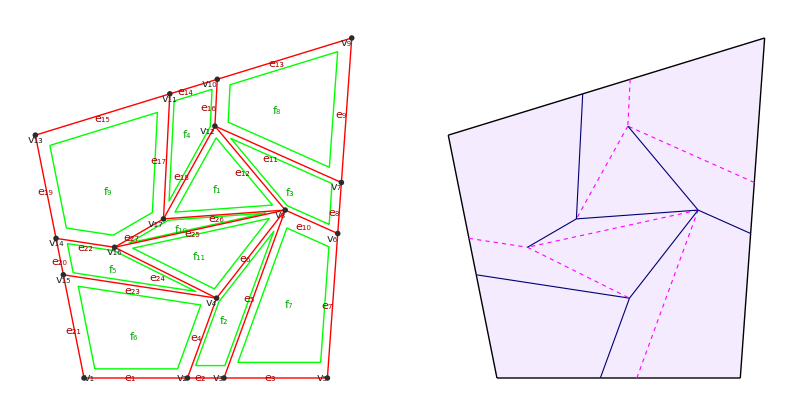

```mathematica
Module[{verts,w,d,τ,ccw,ip,ctype,types,tobj},
verts={{0,0},{1,0},{1.1,1.4},{-0.2,1.0}};
w=0.15;
d=0;
τ=70°;
ccw=τ<π/2;
ip=2;
ctype=M;
types={M,M,V,V};
tobj=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]]
```

Example. A CW offset twist.

```mathematica
Module[{verts,w,d,τ,ccw,ip,ctype,types,tobj},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.14;
d=-.12;
τ=90°;
ccw=d>0;
ip=1;
ctype=M;
types={M,M,V,V};
tobj=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

This example illustrates an example in which two of the twist angles change direction from CCW (<90°) to CW (>90°).

TBD: there’s an error in the crease assignment: two of the creases of the smallest triangle should be mountain. (I think this is related to the change of direction of those two twist angles, so should be an easy fix.)

```mathematica
Module[{verts,w,d,τ,ccw,ip,ctype,types,tobj},
verts=UnitQuadrilateralVertices[{60°,90°,90°,120°},.811,4];
w=0.12;
d=0;
τ=80°;
ccw=τ<90°;
ip=2;
ctype=M;
types={M,V,V,M};
tobj=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

#### Notes

If the crease pattern is flat-foldable (not necessarily the case), then the folded form tile is geometrically similar to a crease pattern tile with different {w, d, τ} parameters, and we can use that fact to compute an equivalent tile for the folded form.

This example computes equivalent {w’, d’, τ’} parameters for a folded form tile. Line OABP is the original tile edge. Line OACP’ is the folded image of the edge. Line OP’ is the folded form tile edge; distances and angles are computed relative to it.

```mathematica
Module[{O,A,B,C,P,Pp,Ap,Bp,τp,soln,ex},
O={0,0};
A={(1-w)/2+d,0};
B={(1+w)/2+d,0};
P={1,0};
C=B+2 w Sin[τ] {-Sin[τ],Cos[τ]};
Pp=P+2 w Sin[τ] {-Sin[τ],Cos[τ]};
Ap=LineInt2D[O,Pp-O,A,U[τ]];
Bp=LineInt2D[O,Pp-O,C,U[τ]];
(* equivalent tilt angle for folded form *)
τp=FullSimplify[ArcTan[(U[τ-π/2].(Pp-O))/(U[τ].(Pp-O))]];
Print["τ' = ",τp];
soln=FullSimplify[Solve[{(1-wp)/2+dp==((Ap-O)⟦1⟧)/((Pp-O)⟦1⟧),(1+wp)/2+dp==((Bp-O)⟦1⟧)/((Pp-O)⟦1⟧)},{wp,dp}]];
Print["w' = ",wp/.soln⟦1⟧,", d' = ",dp/.soln⟦1⟧];
(* and show a plot of the geometry *)
ex={w->0.15,d->-0.08,τ->70°};
Graphics[{
Black,Line[{O,P}],
Gray,Line[{A,A+.5U[τ]}],Line[{B,B+.5U[τ]}],Line[{C,C+.5U[τ]}],
Orange,Line[{O,Pp}],
Green,Line[{A,C,Pp}],
LightGray,Line[{B,C}],Line[{P,Pp}],Line[{C-.1U[τ],C}],
Black,
Point[O],Text["O",O,{2,0}],
Point[A],Text["A",A,{0,2}],
Point[B],Text["B",B,{0,2}],
Point[C],Text["C",C,{0,-2}],
Point[P],Text["P",P,{-2,0}],
Point[Pp],Text["P'",Pp,{-2,0}],
Point[Ap],Text["A'",Ap,{0,-2}],
Point[Bp],Text["B'",Bp,{1,-2}],
{}}]/.ex
]//ShowExample
```

#### RenderTile[{QuadrilateralSplitTwistTile, verts, w, d, τ, ccw, ip, ctype, types}, TGraph2DAssigned, opts] (options) Tolerance

RenderTile[{QuadrilateralSplitTwistTile, verts, w, τ, types}, TGraph2DAssigned, opts] returns a TGraph2DAssigned+TTwistGraph for the folded form of a quadrilateral split twist twist.

It contains Vertices for the CP and Vertices2D for the FF, but note that they are at different relative scale, so as to fit within the same tile. That is, the FF is not actually what you’d get if you folded the CP, but rather, it is the geometrically similar folded form tile.

```mathematica
RenderTile[{QuadrilateralSplitTwistTile,verts_List, w_,d_, τ_,ccw_,ip_,ctype_,types_List},TGraph2DAssigned,opts___] := Module[{tobjcp,tobjff},
tobjcp=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},TGraphAssigned,opts];
tobjff=RenderTile[{QuadrilateralSplitTwistTile,verts,-w/(1-2w),d/(1-2 w),ArcCot[Cot[τ]/(1-2w)],ccw,ip,ctype,types},TGraphAssigned,opts];
tobjcp//AddTGraph2D[tobjff[Vertices]]]
```

Example: a CCW centered twist.

```mathematica
Module[{verts,w,d,τ,ccw,ip,ctype,types,tobj},
verts={{0,0},{1,0},{1.1,1.4},{-0.2,1.0}};
w=0.15;
d=0;
τ=70°;
ccw=τ<π/2;
ip=2;
ctype=M;
types={M,M,V,V};
tobj=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

Example. A CW offset twist.

```mathematica
Module[{verts,w,d,τ,ccw,ip,ctype,types,tobj},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.14;
d=.12;
τ=90°;
ccw=d>0;
ip=1;
ctype=V;
types={M,M,V,M};
tobj=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,τ,ccw,ip,ctype,types},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

### Quadrilateral centered split twist tiles

#### {QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types}

{QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types} is a tiletype that describes a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, 
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
QuadrilateralCenteredSplitTwistTile::usage="QuadrilateralCenteredSplitTwistTile is a tile type that produces an edge-centered split twist from parameters {w, τ} in a polygon.";
```

#### RenderTile[{QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types}, TileVertices, opts] RenderTile[{QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types}, Tiling, opts]

RenderTile[{QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types}, TileVertices, opts] returns the vertices of the tiling polygon.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistTile,verts_List,w_,τ_,ip_,ctype_,types_List},TileVertices,opts___]:=verts
```

Example

```mathematica
Module[{verts,w,τ,ip,ctype,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
τ=70°;
ip=2;
ctype=M;
types={M,M,V,V};
RenderTile[{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types},TileVertices]
]//ShowExample
```

RenderTile[{QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types}, Tiling, opts] returns a rendering of the tiling polygon following the CenteredTwistTile.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistTile,verts_List,w_,τ_,ip_,ctype_,types_List},Tiling,opts___]:=RenderTile[{PolygonCenteredTwistTile,verts,w,τ,types},Tiling,opts]
```

Example: with edge arrows.

```mathematica
Module[{verts,w,τ,ip,ctype,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
τ=70°;
ip=2;
ctype=M;
types={M,M,V,V};
Graphics[RenderTile[{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types},Tiling,TileEdgeArrowStyle->TileArrowCF]]/.TilingStyle[]
]//ShowExample
```

#### RenderTile[{QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types}, TGraphAssigned, opts]

RenderTile[{QuadrilateralCenteredSplitTwistTile, verts, w, τ, ip, ctype, types}, TGraphAssigned, opts] returns a TGraphAssigned+TTwistGraph that describes a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, 
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistTile,verts_List, w_, τ_,ip_,ctype_,types_List},TGraphAssigned,opts___]:=RenderTile[{QuadrilateralSplitTwistTile,verts,w,0,τ,τ<π/2,ip,ctype,types},TGraphAssigned,opts]
```

Examples: TGraphAssigned tile.

```mathematica
Module[{tobj,verts,w,τ,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
τ=75°;
ip=1;
ctype=M;
types={M,M,M,M};
tobj=RenderTile[{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

#### RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TGraph2DAssigned, opts] (options) Tolerance

RenderTile[{PolygonCenteredTwistTile, verts, w, τ, types}, TGraph2DAssigned, opts] returns a TGraph2DAssigned+TTwistGraph for the folded form of a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, 
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistTile,verts_List, w_, τ_,ip_,ctype_,types_List},TGraph2DAssigned,opts___]:=RenderTile[{QuadrilateralSplitTwistTile,verts,w,0,τ,τ<π/2,ip,ctype,types},TGraph2DAssigned,opts]
```

Example: TGraph2DAssigned tile.

```mathematica
Module[{tobj,verts,w,τ,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
τ=75°;
ip=1;
ctype=M;
types={M,M,M,M};
tobj=RenderTile[{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### Crease pattern and folded form

CreasePattern and FoldedForm2D tiles are generated automatically from their respective TGraphAssigned and TGraph2DAssigned tiles.

Example: CreasePattern and FoldedForm2D decorations for an individual tile.

```mathematica
Module[{tobj,verts,w,τ,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
τ=75°;
ip=1;
ctype=M;
types={M,M,M,M};
GraphicsRow[{Graphics[RenderTile[{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types},CreasePattern]],Graphics[RenderTile[{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types},FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

A tiling of two tiles and then render it as tiling, crease pattern, and folded form.

```mathematica
Module[{verts,w,τ,ip,ctype,types,tiling},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
τ=75°;
ip=1;
ctype=M;
types={M,M,V,V};
tiling=JoinTiling[{
{{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types}},
{{QuadrilateralCenteredSplitTwistTile,verts,w,τ,ip,ctype,types},{1,3,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Quadrilateral centered split twist alternate form tiles

#### {QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types}

{QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types} is a tiletype that describes a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	α is the desired twist angle (although the actual twist angle may end up different), 
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
QuadrilateralCenteredSplitTwistAltTile::usage="QuadrilateralCenteredSplitTwistAltTile is a tile type that produces an edge-centered split twist from parameters {w, α} in a polygon.";
```

#### RenderTile[{QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types}, TileVertices, opts] RenderTile[{QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types}, Tiling, opts]

RenderTile[{QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types}, TileVertices, opts] returns the vertices of the tiling polygon.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts_List,w_,α_,ip_,ctype_,types_List},TileVertices,opts___]:=verts
```

Example

```mathematica
Module[{verts,w,α,ip,ctype,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
α=25°;
ip=2;
ctype=M;
types={M,M,V,V};
RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types},TileVertices]
]//ShowExample
```

RenderTile[{QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types}, Tiling, opts] returns a rendering of the tiling polygon following the PolygonCenteredTwistAlt.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts_List,w_,α_,ip_,ctype_,types_List},Tiling,opts___]:=RenderTile[{PolygonCenteredTwistAltTile,verts,w,α,types},Tiling,opts]
```

Example: with edge arrows.

```mathematica
Module[{verts,w,α,ip,ctype,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
α=70°;
ip=2;
ctype=M;
types={M,M,V,V};
Graphics[RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types},Tiling,TileEdgeArrowStyle->TileArrowCF]]/.TilingStyle[]
]//ShowExample
```

#### RenderTile[{QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types}, TGraphAssigned, opts]

RenderTile[{QuadrilateralCenteredSplitTwistAltTile, verts, w, α, ip, ctype, types}, TGraphAssigned, opts] returns a TGraphAssigned+TTwistGraph that describes a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	α is the desired twist angle,
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts_List, w_, α_,ip_,ctype_,types_List},TGraphAssigned,opts___]:=RenderTile[{QuadrilateralSplitTwistTile,verts,w,0,CenteredTwistTiltAngle[w,α],α<π/2,ip,ctype,types},TGraphAssigned,opts]
```

Examples: TGraphAssigned tile.

```mathematica
Module[{tobj,verts,w,α,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
α=30°;
ip=1;
ctype=M;
types={M,M,M,M};
tobj=RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

#### RenderTile[{PolygonCenteredTwistTile, verts, w, α, types}, TGraph2DAssigned, opts] (options) Tolerance

RenderTile[{PolygonCenteredTwistTile, verts, w, α, types}, TGraph2D, opts] returns a TGraph2DAssigned+TTwistGraph for the folded form of a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	α is the desired twist angle,
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts_List, w_, α_,ip_,ctype_,types_List},TGraph2DAssigned,opts___]:=RenderTile[{QuadrilateralSplitTwistTile,verts,w,0,CenteredTwistTiltAngle[w,α],α<π/2,ip,ctype,types},TGraph2DAssigned,opts]
```

Example: TGraph2DAssigned tile.

```mathematica
Module[{tobj,verts,w,α,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
α=30°;
ip=1;
ctype=M;
types={M,M,M,M};
tobj=RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### Crease pattern and folded form

CreasePattern and FoldedForm2D tiles are generated automatically from their respective TGraphAssigned and TGraph2DAssigned tiles.

Example: CreasePattern and FoldedForm decorations for an individual tile.

```mathematica
Module[{tobj,verts,w,α,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
α=30°;
ip=1;
ctype=M;
types={M,M,M,M};
GraphicsRow[{Graphics[RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types},CreasePattern]],Graphics[RenderTile[{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types},FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

A tiling of two tiles and then render it as tiling, crease pattern, and folded form.

```mathematica
Module[{verts,w,α,ip,ctype,types,tiling},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
α=30°;
ip=1;
ctype=M;
types={M,M,V,V};
tiling=JoinTiling[{
{{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types}},
{{QuadrilateralCenteredSplitTwistAltTile,verts,w,α,ip,ctype,types},{1,3,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Quadrilateral offset split twist tiles

#### {QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types}

{QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types} is a tiletype that describes a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	d is the offset,
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
QuadrilateralOffsetSplitTwistTile::usage="QuadrilateralOffsetSplitTwistTile is a tile type that produces an offset split twist from parameters {w, d} in a polygon.";
```

#### RenderTile[{QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types}, TileVertices, opts] RenderTile[{QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types}, Tiling, opts]

RenderTile[{QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types}, TileVertices, opts] returns the vertices of the tiling polygon.

```mathematica
RenderTile[{QuadrilateralOffsetSplitTwistTile,verts_List,w_,d_,ip_,ctype_,types_List},TileVertices,opts___]:=verts
```

Example

```mathematica
Module[{verts,w,d,ip,ctype,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=0.1;
ip=2;
ctype=M;
types={M,M,V,V};
RenderTile[{QuadrilateralOffsetSplitTwistTile,verts,w,d,ip,ctype,types},TileVertices]
]//ShowExample
```

RenderTile[{QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types}, Tiling, opts] returns a rendering of the tiling polygon following the PolygonOffsetTwistTile.

```mathematica
RenderTile[{QuadrilateralOffsetSplitTwistTile,verts_List,w_,d_,ip_,ctype_,types_List},Tiling,opts___]:=RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},Tiling,opts]
```

Example: with fill and arrows.

```mathematica
Module[{verts,w,d,ip,ctype,types},
verts=UnitRegularPolygonVertices[4];
w=0.2;
d=70°;
ip=2;
ctype=M;
types={M,M,V,V};
Graphics[RenderTile[{QuadrilateralOffsetSplitTwistTile,verts,w,d,ip,ctype,types},Tiling,TilePolys->True, TileEdgeArrowStyle->TileArrowDF]]/.TilingStyle[]
]//ShowExample
```

#### RenderTile[{QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types}, TGraphAssigned, opts]

RenderTile[{QuadrilateralOffsetSplitTwistTile, verts, w, d, ip, ctype, types}, TGraphAssigned, opts] returns a TGraphAssigned+TTwistGraph that describes a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	d is the offset,
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{QuadrilateralOffsetSplitTwistTile,verts_List, w_, d_,ip_,ctype_,types_List},TGraphAssigned,opts___]:=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,90°,d>0,ip,ctype,types},TGraphAssigned,opts]
```

Examples: TGraph tile.

```mathematica
Module[{tobj,verts,w,d,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
d=0.1;
ip=1;
ctype=M;
types={M,M,M,M};
tobj=RenderTile[{QuadrilateralOffsetSplitTwistTile,verts,w,d,ip,ctype,types},TGraphAssigned];
GraphicsRow[{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}]]/.OrigamiStyle[]//ShowExample
```

#### RenderTile[{PolygonCenteredTwistTile, verts, w, d, types}, TGraph2DAssigned, opts] (options) Tolerance

RenderTile[{PolygonCenteredTwistTile, verts, w, d, types}, TGraph2DAssigned, opts] returns a TGraph2DAssigned+TTwistGraph for the folded form of a split twist in a quadrilateral specified by its vertices verts where 
	w is the fractional width of each pleat where it subtends its edge, 
	d is the offset,
	ip is the index of the vertex to preserve,
	ctype is the fold type of the crossing fold,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
RenderTile[{QuadrilateralOffsetSplitTwistTile,verts_List, w_, d_,ip_,ctype_,types_List},TGraph2DAssigned,opts___]:=RenderTile[{QuadrilateralSplitTwistTile,verts,w,d,90°,d>0,ip,ctype,types},TGraph2DAssigned,opts]
```

Example: TGraph2DAssigned tile.

```mathematica
Module[{tobj,verts,w,d,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
d=0.1;
ip=1;
ctype=M;
types={M,M,M,M};
tobj=RenderTile[{QuadrilateralOffsetSplitTwistTile,verts,w,d,ip,ctype,types},TGraph2DAssigned];
GraphicsGrid[{{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]},{
Graph2DGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.OrigamiStyle[]
]//ShowExample
```

#### Crease pattern and folded form

CreasePattern and FoldedForm2D tiles are generated automatically from their respective TGraphAssigned and TGraph2DAssigned tiles.

Example: CreasePattern and FoldedForm2D tiles for an individual tile.

```mathematica
Module[{tobj,verts,w,d,ip,ctype,types},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
d=0.1;
ip=1;
ctype=M;
types={M,M,M,M};
GraphicsRow[{Graphics[RenderTile[{QuadrilateralOffsetSplitTwistTile,verts,w,d,ip,ctype,types},CreasePattern]],Graphics[RenderTile[{QuadrilateralOffsetSplitTwistTile,verts,w,d,ip,ctype,types},FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

A tiling of two tiles and then render it as tiling, crease pattern, and folded form.

```mathematica
Module[{verts,w,d,ip,ctype,types,tiling},
verts={{0,0},{1,0},{.9,.8},{.2,1}};
w=0.2;
d=0.1;
ip=1;
ctype=M;
types={M,M,M,M};
tiling=JoinTiling[{
{{QuadrilateralOffsetSplitTwistTile,verts,w,d,ip,ctype,types}},
{{QuadrilateralOffsetSplitTwistTile,verts,w,-d,ip,ctype,types},{1,3,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

Here’s another example, using silver rectangle tiles with offset split twists that gives a woven-like appearance. Note that ip is different for the two tiles.

```mathematica
Module[{verts,w,d,ip,ctype,types,tiling},
verts={{0,0},{1,0},{1,1/√2},{0,1/√2}};
w=0.2;
d=0.12;
ip=1;
ctype=V;
types={V,V,V,V};
tiling=JoinTiling[{
{{QuadrilateralOffsetSplitTwistTile,verts,w,d,1,ctype,types}},
{{QuadrilateralOffsetSplitTwistTile,verts,w,-d,4,ctype,types},{1,3,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

## Monolithic tilings

### Monolithic graphs

#### Notes

Normally when you create the CreasePattern or FoldedForm decorations, they are composed of many separate units that only look like they’re one big thing because both CP and FF extends precisely to the tile polygon boundaries and no further. This ends up looking fine in the interior of the pattern (usually), but that means that the edge of the paper may be incorrectly rendered in the folded form, since folded form tiles are usually not precisely the exact folded form of a crease pattern tile.

If we want to render the folded form precisely so that it matches the crease pattern, then we should use one of the functions in this section, which merge individual tiles together into a single monolithic TGraphAssigned, TGraph2DAssigned, or TGraph3DAssigned, and then create the crease pattern or folded form from that.

This guarantees that the rendered folded form is correctly the folded form of the individual tiling. However, the merging process is costly (in terms of time).

Note that this process can be used to create folded form renderings of tilings where the individual tiles are not geometrically similar to their folded forms. It effectively simulates the manual process of creating a tiling-based tessellation; we create crease pattern tiles, glue them together, then fold up the result.

You can accomplish the same thing without going through the Tiling infrastructure by using the functions MergeGraphs and JoinGraphs (and their descendants) directly if you are putting together small numbers of folded shapes.

#### MonolithicEmbedTiling[tiling, decoration, opts] (options) KillMergedEdges, SamePtTolerance, CollinearCleanup, CollinearTolerance

MonolithicEmbedTiling[tiling, decoration, opts] embeds a tiling as a single TGraph (or descendant) object by merging individual tiles.

Arguments:
	tiling — a tiling
	decoration — one of TGraphAssigned, TGraph2DAssigned, or TGraph3DAssigned.

Options:
	KillMergedEdges → True | False, specify whether to remove borders edges of tiles.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.
	CollinearCleanup → True | False, specify whether to remove degree-2 vertices between collinear edges.
	CollinearTolerance → tol, tolerance on whether two edges at degree-2 vertices are collinear.

Returns a single TGraph+TAssigned descendant containing the merged graph.

```mathematica
MonolithicEmbedTiling::baddec="`1` is an invalid decoration for MonolithicEmbedTiling.";
```

```mathematica
CollinearCleanup::usage="CollinearCleanup is an option to MonolithicEmbedTiling that specifies whether to remove degree-2 vertices between collinear edges.";
```

```mathematica
Options[MonolithicEmbedTiling]={
KillMergedEdges->True,
CollinearCleanup->True
};
```

If we haven’t implemented a decoration, throw an error.

```mathematica
MonolithicEmbedTiling[tiling_List,decoration_,opts___]:=(Message[MonolithicEmbedTiling::baddec,decoration];Abort[]);
```

#### MonolithicEmbedTiling[tiling, TGraphAssigned, opts] (options) KillMergedEdges, SamePtTolerance, CollinearCleanup, CollinearTolerance

MonolithicEmbedTiling[tiling, TGraphAssigned, opts] embeds a tiling as a single TGraphAssigned by merging individual tiles.

Options:
	KillMergedEdges → True | False, specify whether to remove borders edges of tiles.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.
	CollinearCleanup → True | False, specify whether to remove degree-2 vertices between collinear edges.
	CollinearTolerance → tol, tolerance on whether two edges at degree-2 vertices are collinear.

```mathematica
MonolithicEmbedTiling[tiling_List,TGraphAssigned,opts___]:=Module[{cc,kme,tlist,tobj},
kme=KillMergedEdges/.{opts}/.Options[MonolithicEmbedTiling];
cc=CollinearCleanup/.{opts}/.Options[MonolithicEmbedTiling];
tlist=EmbedTiling[tiling,TGraphAssigned];
tobj=MergeGraphAssigneds[tlist,KillMergedEdges->kme,opts];
If[cc,tobj=CollinearCleanupGraphAssigned[tobj]];
tobj//RebuildPlaneGraph]
```

Example.

```mathematica
Module[{w,α,name,verts,tiling,tobj,tobj1},
w=0.18;
α=30°;
name=PolygonCenteredTwistAltTile;
verts=UnitRegularPolygonVertices[4];
tiling=JoinTiling[{
{{name,verts,w,α,{V,V,V,V}}},
{{name,verts,w,α,{M,M,M,M}},{1,2,1}},
{{name,verts,w,α,{M,M,M,M}},{1,3,2}},
{{name,verts,w,α,{V,V,V,V}},{2,3,2}}
}];
tobj=MonolithicEmbedTiling[tiling,TGraphAssigned];
GraphicsGrid[{{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]]},{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### MonolithicEmbedTiling[tiling, TGraph2DAssigned, opts] (options) StationaryFace, KillMergedEdges, SamePtTolerance, CollinearCleanup, CollinearTolerance

MonolithicEmbedTiling[tiling, TGraph2DAssigned, opts] embeds a tiling as a single TGraph2DAssigned by merging individual tiles. Its folded form is the actual folded form resulting from folding the tiles.

Options:
	StationaryFace → sface is passed through to FoldGraph2D.
	KillMergedEdges → True | False, specify whether to remove borders edges of tiles.
	SamePtTolerance → tol, tolerance on whether two vertices are distinct.
	CollinearCleanup → True | False, specify whether to remove degree-2 vertices between collinear edges.
	CollinearTolerance → tol, tolerance on whether two edges at degree-2 vertices are collinear.

```mathematica
MonolithicEmbedTiling[tiling_List,TGraph2DAssigned,opts___]:=Module[{cc,kme,tlist,tobj},
kme=KillMergedEdges/.{opts}/.Options[MonolithicEmbedTiling];
cc=CollinearCleanup/.{opts}/.Options[MonolithicEmbedTiling];
tlist=EmbedTiling[tiling,TGraph2DAssigned];
tobj=MergeGraph2DAssigneds[tlist,KillMergedEdges->kme,opts];
If[cc,tobj=CollinearCleanupGraph2DAssigned[tobj]];
tobj=tobj//RebuildPlaneGraph;
FoldGraph2D[tobj,TypeToFlatFoldAngle[tobj[EdgeTypes]],opts]]
```

Example.

```mathematica
Module[{w,α,name,verts,tiling,tobj,tobj1},
w=0.18;
α=30°;
name=PolygonCenteredTwistAltTile;
verts=UnitRegularPolygonVertices[4];
tiling=JoinTiling[{
{{name,verts,w,α,{V,V,V,V}}},
{{name,verts,w,α,{M,M,M,M}},{1,2,1}},
{{name,verts,w,α,{M,M,M,M}},{1,3,2}},
{{name,verts,w,α,{V,V,V,V}},{2,3,2}}
}];
tobj=MonolithicEmbedTiling[tiling,TGraph2DAssigned];
GraphicsGrid[{{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]],Graphics[EmbedTiling[tiling,FoldedForm2D]]},{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj]}}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Monolithic graphs, crease patterns, and folded form, backwards compatible

#### Notes

In Tessellatica 11.0, we generated monolithic graphs, CPs, and FFs using different calling functions. We here map the old calling functions to our new ones to make it easier to port old examples.

Everything in this section is deprecated; you should call MonolithicEmbedTiling directly with the appropriate decoration.

#### Tiling decorations MonolithicTGraph, MonolithicTGraph2D, MonolithicCreasePattern, MonolithicFoldedForm

```mathematica
MonolithicTGraph::usage="MonolithicTGraph is a type of tile decoration that renders the full tiling as a single TGraph.";
```

```mathematica
MonolithicTGraph2D::usage="MonolithicTGraph2D is a type of tile decoration that renders the full tiling as a single TGraph2D.";
```

```mathematica
MonolithicCreasePattern::usage="MonolithicCreasePattern is a type of tile decoration that renders the full tiling as a single crease pattern.";
```

```mathematica
MonolithicFoldedForm::usage="MonolithicFoldedForm is a type of tile decoration that renders the full tiling as a single folded form.";
```

#### EmbedTiling[tiling, MonolithicTGraph, opts]

EmbedTiling[tiling, MonolithicTGraph, opts] joins the individual tiles together into a single TGraph.

```mathematica
EmbedTiling[tiling_List,MonolithicTGraph,opts___]:=MonolithicEmbedTiling[tiling,TGraphAssigned,opts]
```

Example

```mathematica
Module[{w,α,name,verts,tiling,tobj},
w=0.18;
α=30°;
name=PolygonCenteredTwistAltTile;
verts=UnitRegularPolygonVertices[4];
tiling=JoinTiling[{
{{name,verts,w,α,{V,V,V,V}}},
{{name,verts,w,α,{M,M,M,M}},{1,2,1}},
{{name,verts,w,α,{M,M,M,M}},{1,3,2}},
{{name,verts,w,α,{V,V,V,V}},{2,3,2}}
}];
tobj=EmbedTiling[tiling,MonolithicTGraph];
GraphicsGrid[{{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]]},{
GraphGraphics[tobj],
CreasePatternGraphics[tobj]}}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### EmbedTiling[tiling, MonolithicTGraph2D, opts] (options) StationaryFace

EmbedTiling[tiling, MonolithicTGraph2D, opts] joins the individual tiles together into a single TGraph, then folds it into a TGraph2D. Options are:
	StationaryFace → sface is passed through to FoldGraph2D.

```mathematica
EmbedTiling[tiling_List,MonolithicTGraph2D,opts___]:=MonolithicEmbedTiling[tiling,TGraph2DAssigned,opts]
```

Example

```mathematica
Module[{w,α,name,verts,tiling,tobj},
w=0.18;
α=30°;
name=PolygonCenteredTwistAltTile;
verts=UnitRegularPolygonVertices[4];
tiling=JoinTiling[{
{{name,verts,w,α,{V,V,V,V}}},
{{name,verts,w,α,{M,M,M,M}},{1,2,1}},
{{name,verts,w,α,{M,M,M,M}},{1,3,2}},
{{name,verts,w,α,{V,V,V,V}},{2,3,2}}
}];
tobj=EmbedTiling[tiling,MonolithicTGraph2D,StationaryFace->3];
GraphicsGrid[{{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]},{
GraphGraphics[tobj],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->3]}}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### EmbedTiling[tiling, MonolithicCreasePattern, opts]

EmbedTiling[tiling, MonolithicCreasePattern, opts] joins the individual tiles together into a single crease pattern.

```mathematica
EmbedTiling[tiling_List,MonolithicCreasePattern,opts___]:=CreasePatternGraphics[EmbedTiling[tiling,MonolithicTGraph,opts]]
```

Example

```mathematica
Module[{w,α,name,verts,tiling,tobj},
w=0.18;
α=30°;
name=PolygonCenteredTwistAltTile;
verts=UnitRegularPolygonVertices[4];
tiling=JoinTiling[{
{{name,verts,w,α,{V,V,V,V}}},
{{name,verts,w,α,{M,M,M,M}},{1,2,1}},
{{name,verts,w,α,{M,M,M,M}},{1,3,2}},
{{name,verts,w,α,{V,V,V,V}},{2,3,2}}
}];
tobj=EmbedTiling[tiling,MonolithicTGraph];
GraphicsGrid[{{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]]},{
GraphGraphics[tobj],
Graphics[EmbedTiling[tiling,MonolithicCreasePattern]]}}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### EmbedTiling[tiling, MonolithicFoldedForm, opts] (options) StationaryFace, FaceupFace

EmbedTiling[tiling, MonolithicFoldedForm, opts] joins the individual tiles together into a single TGraph2D, then returns the VisibleFoldedFormGraphics. Options are:
	StationaryFace → sface is passed through to FoldGraph2D.
	FaceupFace → fuface is passed through to VisibleFoldedFormGraphics.

```mathematica
EmbedTiling[tiling_List,MonolithicFoldedForm,opts___]:=VisibleFoldedFormGraphics[EmbedTiling[tiling,MonolithicTGraph2D,opts],opts]
```

Example

```mathematica
Module[{w,α,name,verts,tiling,tobj},
w=0.18;
α=30°;
name=PolygonCenteredTwistAltTile;
verts=UnitRegularPolygonVertices[4];
tiling=JoinTiling[{
{{name,verts,w,α,{V,V,V,V}}},
{{name,verts,w,α,{M,M,M,M}},{1,2,1}},
{{name,verts,w,α,{M,M,M,M}},{1,3,2}},
{{name,verts,w,α,{V,V,V,V}},{2,3,2}}
}];
tobj=EmbedTiling[tiling,MonolithicTGraph2D,StationaryFace->3];
GraphicsGrid[{{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]},{
GraphGraphics[tobj],
Graphics[EmbedTiling[tiling,MonolithicCreasePattern]],
Graphics[EmbedTiling[tiling,MonolithicFoldedForm,StationaryFace->3,FaceupFace->3]]}}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

## Unit polygon tiles

#### Notes

All of the tiles in this section are unit polygons, polygons whose first vertex is at {0,0}, second at {1,0}, and the tile lies in the upper half plane. Instead of being specified by their tile vertices, they are specified by a smaller number of parameters, which are different for each type of tile. This permits a very concise description of tilings composed of regular polygons.

### Unit regular polygon tiles

#### {UnitRegularPolygonTile, n}

{UnitRegularPolygonTile, n} is a tiletype that specifies a unit regular n-gon.

```mathematica
UnitRegularPolygonTile::usage="UnitRegularPolygonTile is a tile type that produces a unit regular polygon.";
```

#### RenderTile[{UnitRegularPolygonTile, n}, decoration, opts]

RenderTile[{UnitRegularPolygonTile, n}, decoration, opts] renders the tile as a PolygonTile for any decoration.

```mathematica
RenderTile[{UnitRegularPolygonTile, n_},decoration_,opts___]:=RenderTile[{PolygonTile,UnitRegularPolygonVertices[n]},decoration,opts]
```

Example

```mathematica
Graphics[RenderTile[{UnitRegularPolygonTile,5},Tiling]]/.TilingStyle[]//ShowExample
```

### Unit regular polygon centered twist properties

#### UnitRegularPolygonCenteredTwistSelfContainedQ[n, w, τ, types]

UnitRegularPolygonCenteredTwistSelfContainedQ[n, w, τ, types] returns True if the angles and MV-assignment are consistent with a valid simple flat twist AND the resulting tile is self-contained, meaning that the twist polygon ends up wholly contained by its tile.

```mathematica
UnitRegularPolygonCenteredTwistSelfContainedQ[n_,w_,τ_,types_List]:=RegularPolygonTwistValidQ[n,CenteredTwistAngle[w,τ],types]&&Abs[Tan[τ]]>Tan[π/n]/(1-2w);
```

#### UnitRegularPolygonCenteredTwistSelfContainedTypes[n, w, τ]

UnitRegularPolygonCenteredTwistSelfContainedTypes[n, w, τ] returns a list of all MV-assigments that produce valid self-contained unit polygon twist tiles for the given parameters.

```mathematica
UnitRegularPolygonCenteredTwistSelfContainedTypes[n_,w_,τ_]:=Select[AllCyclicTwistTypes[n],UnitRegularPolygonCenteredTwistSelfContainedQ[n,w,τ,#]&]
```

### Unit regular polygon centered twist tiles

#### {UnitRegularPolygonCenteredTwistTile, n, w, τ, types}

{UnitRegularPolygonCenteredTwistTile, n, w, τ, types} represents an edge-centered simple flat twist in a unit n-gon where w is the width of the pleat where it subtends the edge, τ is the pleat angle, defined as the rotation angle of the pleat measured with respect to the edge, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitRegularPolygonCenteredTwistTile::usage="UnitRegularPolygonCenteredTwistTile is a tile type that produces an edge-centered simple flat twist from parameters {w, τ} in a regular unit polygon.";
```

#### RenderTile[{UnitRegularPolygonCenteredTwistTile, n, w, τ, types}, decoration, opts]

RenderTile[{UnitRegularPolygonCenteredTwistTile, n, w, τ}, decoration, opts] renders the tile as a PolygonCenteredTwistTile for any decoration.

```mathematica
RenderTile[{UnitRegularPolygonCenteredTwistTile,n_,w_,τ_,types_List},decoration_,opts___]:=RenderTile[{PolygonCenteredTwistTile,UnitRegularPolygonVertices[n],w,τ,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{n,w,τ,types,tiling},
n=4;
w=0.2;
τ=70°;
types={M,M,V,V};
tiling={
{{UnitRegularPolygonCenteredTwistTile,n,w,τ,types}},
{{UnitRegularPolygonCenteredTwistTile,n,w,τ,types},{0,1}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit regular polygon centered twist alternate form properties

#### UnitRegularPolygonCenteredTwistAltSelfContainedQ[n, w, α, types]

UnitRegularPolygonCenteredTwistAltSelfContainedQ[n, w, α, types] returns True if the angles and MV-assignment are consistent with a valid simple flat twist AND the resulting tile is self-contained, meaning that the twist polygon ends up wholly contained by its tile.

```mathematica
UnitRegularPolygonCenteredTwistAltSelfContainedQ[n_,w_,α_,types_List]:=UnitRegularPolygonCenteredTwistSelfContainedQ[n,w,CenteredTwistTiltAngle[w,α],types]
```

#### UnitRegularPolygonCenteredTwistAltSelfContainedTypes[n, w, α]

UnitRegularPolygonCenteredTwistAltSelfContainedTypes[n, w, α] returns a list of all MV-assigments that produce valid self-contained unit polygon twist tiles for the given parameters.

```mathematica
UnitRegularPolygonCenteredTwistAltSelfContainedTypes[n_,w_,α_]:=Select[AllCyclicTwistTypes[n],UnitRegularPolygonCenteredTwistAltSelfContainedQ[n,w,α,#]&]
```

### Unit regular polygon centered twist alternate form tiles

#### {UnitRegularPolygonCenteredTwistAltTile, n, w, α, types}

{UnitRegularPolygonCenteredTwistAltTile, n, w, α, types} represents an edge-centered simple flat twist in a unit n-gon twist where w is the width of the pleat where it subtends the edge, α is the twist angle, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitRegularPolygonCenteredTwistAltTile::usage="UnitRegularPolygonCenteredTwistAlt is a tile type that produces an edge-centered simple flat twist from parameters {w, α} in a regular unit polygon.";
```

#### RenderTile[{UnitRegularPolygonCenteredTwistAltTile, n, w, α, types}, decoration, opts]

RenderTile[{UnitRegularPolygonCenteredTwistAltTile, n, w, α}, decoration, opts] renders the tile as a PolygonCenteredTwistTile for any decoration.

```mathematica
RenderTile[{UnitRegularPolygonCenteredTwistAltTile,n_,w_,α_,types_List},decoration_,opts___]:=RenderTile[{PolygonCenteredTwistAltTile,UnitRegularPolygonVertices[n],w,α,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{n,w,α,types,tiling},
n=4;
w=0.2;
α=30°;
types={M,M,V,V};
tiling={
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types}},
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types},{0,1}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit regular polygon offset twist properties

#### Notes

These functions implement offset twists (pleats perpendicular to the tile edges) in unit regular polygons.

This example computes and plots the vertices of three consecutive edges, symbolically on n, from which we can compute symbolic expressions for the twist angle, shrinkage, and rotation.

```mathematica
Module[{c,v,r,s,q},
c=UnitRegularPolygonCenter[n];
v[i_]:=c-RotationMatrix2D[2π(i-1)/n].c;
r[i_]:=((1+w)/2-d)v[i]+((1-w)/2+d)v[i+1];
s[i_]:=((1-w)/2-d)v[i]+((1+w)/2+d)v[i+1];
q[i_]:=LineInt2D[s[i-1],U[2π(i-2)/n+π/2],r[i],U[2π(i-1)/n+π/2]];
Print["Twist angle = ",FullSimplify[ArcTan[w/((q[2]-q[1])⟦2⟧)]]];
Print["Shrinkage = ",FullSimplify[Mag[q[2]-q[1]]]];
Print["Rotation = ",FullSimplify[ArcTan[((q[2]-q[1])⟦2⟧)/w]]];
Graphics[{
Style[Line[{v[0],v[1],v[2],v[3]}],Black],
Style[{Line[{s[0],q[1],r[1]}],Line[{s[1],q[2],r[2]}]},Blue],
Style[Line[{q[0],q[1],q[2],q[3]}],Red]
},Frame->True]/.{n->5,w->0.2,d->0.1}
]//ShowExample
```

#### UnitRegularPolygonOffsetTwistAngle[n, w, d] UnitRegularPolygonOffsetTwistOffset[n, w, α]

UnitRegularPolygonOffsetTwistAngle[n, w, d] returns the twist angle α for a unit polygon offset twist of order n, pleat width w, and offset d.

```mathematica
UnitRegularPolygonOffsetTwistAngle[n_,w_,d_]:=Mod[ArcTan[w/(2d)Cot[π/n]],π]
```

UnitRegularPolygonOffsetTwistOffset[n,w,α] returns the offset parameter d for a unit polygon offset twist of order n, pleat width w, and twist angle α.

```mathematica
UnitRegularPolygonOffsetTwistOffset[n_,w_,α_]:=w/2 Cot[π/n]Cot[α]
```

The important thing to note here is that tile mating happens for constant w, d, so α is going to vary from tile to tile (if the number of sides, n, is different). This example plot shows that, in general, the twist angle gets larger for increasing n.

```mathematica
Module[{w,d,pts},
w=0.2;
d=0.2;
pts=Table[{n,UnitRegularPolygonOffsetTwistAngle[n,w,d]/°},{n,3,12}];
ListPlot[pts,PlotRange->{{0,12},{0,90}},AxesLabel->{"n","α/°"}]
]//ShowExample
```

#### UnitRegularPolygonOffsetTwistSelfContainedQ[n, w, d, types] UnitRegularPolygonOffsetTwistAltSelfContainedQ[n, w, α, types]

UnitRegularPolygonOffsetTwistSelfContainedQ[n, w, d, types] returns True if the angles and MV-assignment are consistent with a valid simple flat twist AND the resulting tile is self-contained, i.e., the twist polygon lies wholly within its tile.

```mathematica
UnitRegularPolygonOffsetTwistSelfContainedQ[n_,w_,d_,types_List]:=RegularPolygonTwistValidQ[n,UnitRegularPolygonOffsetTwistAngle[n,w,d],types]&&w≤1/3(1-2Abs[d]);
```

UnitRegularPolygonOffsetTwistAltSelfContainedQ[n, w, α, types] returns the same thing but using twist angle α.

```mathematica
UnitRegularPolygonOffsetTwistAltSelfContainedQ[n_,w_,α_,types_List]:=UnitRegularPolygonOffsetTwistSelfContainedQ[n,w,UnitRegularPolygonOffsetTwistOffset[n,w,α],types]
```

### Unit regular polygon offset twist tiles

#### {UnitRegularPolygonOffsetTwistTile, n, w, d, types}

{UnitRegularPolygonOffsetTwistTile, n, w, d, types} represents an edge-centered simple flat twist in a unit n-gon where w is the width of the pleat where it subtends the edge, d is the pleat angle, defined as the rotation angle measured with respect to the edge, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitRegularPolygonOffsetTwistTile::usage="UnitRegularPolygonOffsetTwistTile is a tile type that produces an offset simple flat twist from parameters {w, d} in a regular unit polygon.";
```

#### RenderTile[{UnitRegularPolygonOffsetTwistTile, n, w, d, types}, decoration, opts]

RenderTile[{UnitRegularPolygonOffsetTwistTile, n, w, d}, decoration, opts] renders the tile as a PolygonOffsetTwistTile for any decoration.

```mathematica
RenderTile[{UnitRegularPolygonOffsetTwistTile,n_,w_,d_,types_List},decoration_,opts___]:=RenderTile[{PolygonOffsetTwistTile,UnitRegularPolygonVertices[n],w,d,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{n,w,d,types1,types2,tiling},
n=4;
w=0.2;
d=0.15;
types1={V,V,V,V};
types2={V,V,V,V};
tiling={
{{UnitRegularPolygonOffsetTwistTile,n,w,d,types1}},
{{UnitRegularPolygonOffsetTwistTile,n,w,-d,types2},{0,1}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit triangle tiles

#### Notes

There are regular polygons that make nice tilings if you combine them with triangles. Here we define a general unit triangle tile. Triangles in tilings are usually specified by their angles, rather than side length, so that’s what we’ll use here.

#### {UnitTriangleTile, angles}

{UnitTriangleTile, angles} is a tile type that specifies a unit triangle by its corner angles.

```mathematica
UnitTriangleTile::usage="UnitRegularPolygonTile is a tile type that produces a unit triangle.";
```

#### RenderTile[{UnitTriangleTile, angles}, decoration, opts]

RenderTile[{UnitTriangleTile, angles}, decoration, opts] renders the tile as a PolygonTile for any decoration.

```mathematica
RenderTile[{UnitTriangleTile, angles_},decoration_,opts___]:=RenderTile[{PolygonTile,UnitTriangleVertices[angles]},decoration,opts]
```

Example

```mathematica
Graphics[RenderTile[{UnitTriangleTile,{50°,60°,70°}},Tiling]]/.TilingStyle[]//ShowExample
```

### Unit triangle centered twist tiles

#### Notes

Unit triangle tiles can be specified by a list of their three angles. For non-equilateral triangles, the side lengths are, of course, not all equal, and when you start putting them together, you may well wish to scale them. For that, you can use the scale argument in the tilespec.

#### {UnitTriangleCenteredTwistTile, angles, w, τ, types}

{UnitTriangleCenteredTwistTile, angles, w, τ, types} represents an edge-centered simple flat twist in a unit triangle with corner angles angles where w is the width of the pleat where it subtends the edge, τ is the pleat angle, defined as the rotation angle measured with respect to the edge, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitTriangleCenteredTwistTile::usage="UnitTriangleCenteredTwistTile is a tile type that produces an edge-centered simple flat twist from parameters {w, τ} in a unit triangle.";
```

#### RenderTile[{UnitTriangleCenteredTwistTile, angles, w, τ, types}, decoration, opts]

RenderTile[{UnitTriangleCenteredTwistTile, angles, w, τ, types}, decoration, opts] renders the tile as a PolygonCenteredTwistTile for any decoration.

```mathematica
RenderTile[{UnitTriangleCenteredTwistTile,angles_,w_,τ_,types_List},decoration_,opts___]:=RenderTile[{PolygonCenteredTwistTile,UnitTriangleVertices[angles],w,τ,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,w,τ,types1,types2,tiling},
angles={50°,60°,70°};
w=0.1;
τ=80°;
types1={M,M,M};
types2={V,V,V};
tiling=JoinTiling[{
{{UnitTriangleCenteredTwistTile,angles,w,τ,types1}},
{{UnitTriangleCenteredTwistTile,angles,w,τ,types2},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit triangle centered twist alternate form tiles

#### {UnitTriangleCenteredTwistAltTile, angles, w, α, types}

{UnitTriangleCenteredTwistAltTile, angles, w, α, types} represents an edge-centered simple flat twist in a unit triangle with corner angles angles where w is the width of the pleat where it subtends the edge, α is the twist angle, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitTriangleCenteredTwistAltTile::usage="UnitTriangleCenteredTwistAlt is a tile type that produces an edge-centered simple flat twist from parameters {w, α} in a unit triangle.";
```

#### RenderTile[{UnitTriangleCenteredTwistAltTile, angles, w, α, types}, decoration, opts]

RenderTile[{UnitTriangleCenteredTwistAltTile, angles, w, α, types}, decoration, opts] renders the tile as a PolygonCenteredTwistTile for any decoration.

```mathematica
RenderTile[{UnitTriangleCenteredTwistAltTile,angles_,w_,α_,types_List},decoration_,opts___]:=RenderTile[{PolygonCenteredTwistAltTile,UnitTriangleVertices[angles],w,α,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,w,α,types1,types2,tiling},
angles={50°,60°,70°};
w=0.1;
α=25°;
types1={M,M,M};
types2={V,V,V};
tiling=JoinTiling[{
{{UnitTriangleCenteredTwistAltTile,angles,w,α,types1}},
{{UnitTriangleCenteredTwistAltTile,angles,w,α,types2},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit triangle offset twist properties

#### Notes

With offset twists, the polygons that give a flat-foldable tile with the offset construction are fewer than with tilted-pleat twists, which worked for any circumscribable polygon. For offset twists, all regular polygons work, and all triangles work. But for higher-order non-regular polygons, circumscribable ones don’t necessarily work. In fact, it’s an open problem of what polygons do work.

One of the differences that shows up even with triangles is that the circumcenter is not the same for the central and outer polygons, which we’ll show in this example.

Here’s an example of a triangle offset twist for which we compare various properties of the outer and central polygon. These demonstrate that the pleat-to-central-polygon angles are the same (same twist angles) and the central polygon is similar to the outer one (same corner angles), but there is not a universal stationary point the way there is for the tilted-pleat twist.

Some of the calculations are done symbolically so we also output explicit expressions for the twist angles. It takes further manipulation to obtain the simpler expression for twist angle below, but we do check their equivalence.

```mathematica
Module[{tverts,tobj,ex,n,verts,pverts,cverts,tas},
tverts=FullSimplify[UnitTriangleVertices[{θ1,θ2,θ3}]/.θ1+θ2->π-θ3];
tobj=RenderTile[{PolygonOffsetTwistTile,tverts,w,d ,{M,M,M}},TGraphAssigned];
ex={θ1->50.°,θ2->60.°,θ3->70.°,w->0.1,d->0.06};
n=Length[tobj[Faces]⟦tobj[TwistFaces]⟦1⟧⟧];
verts=tobj[Vertices];
pverts=verts⟦{1,5,9}⟧;(* outer polygon vertices *)
cverts=verts⟦{4,8,12}⟧;(* central polygon vertices *)
Print[Graphics[{
Style[Line[Append[pverts,pverts⟦1⟧]],LightGray],
GraphGraphics[tobj]⟦1⟧}]/.ex/.OrigamiStyle[]];
Print["critical twist angles/° = ",TriangleCriticalTwistAngles[{θ1,θ2,θ3}]/°/.ex];
(* directly computed twist angles *)
(* all three twist angles *)
tas=RotationAngle[verts⟦#⟦1⟧⟧-verts⟦#⟦2⟧⟧,verts⟦#⟦3⟧⟧-verts⟦#⟦2⟧⟧]&/@Mod[Table[{4,8,3}+4i,{i,0,n-1}],4n,1]/.ArcTan[x_,y_]:>ArcTan[y/x];
tas=FullSimplify[tas];
Print["Twist angles = ",tas];
Print["Twist angles/° = ",tas/°/.ex];
(* Check our alternate formula for the twist angle *)
Print["check: ",Chop[(tas⟦1⟧-ArcTan[(w/(2d))((Sin[θ1]Sin[θ2]Sin[θ3])/(1+Cos[θ1]Cos[θ2]Cos[θ3]))])/.ex]];
(* Triangle angles (same) *)
Print["Corner angles/°: outer = ",(TriangleAngles2D@@pverts)/°/.ex," inner = ",(TriangleAngles2D@@cverts)/° /.ex];
(* Triangle circumcenters (different) *)
Print["Circumcenters: outer = ",Circumcenter[pverts]/.ex," inner = ",Circumcenter[cverts]/.ex ];
(* Triangle incenters (different) *)
Print["Incenters: outer = ",TriangleIncenter2D@@pverts/.ex," inner = ",TriangleIncenter2D@@cverts /.ex];
(* Triangle Brocard points (different) *)
(* Triangle Brocard points *)
(* Print["Brocard points: outer = ",BrocardTriangleInfo[pverts/.ex]⟦2⟧," inner = ",BrocardTriangleInfo[cverts/.ex]⟦2⟧ ];*)
(* Fixed point of the transformation *)
ctr=ScaleRotationOffsetFixedPoint[Take[pverts,2]/.ex,Take[cverts,2]/.ex];
Print["Fixed point of twist = ",ctr/.ex];
]//ShowExample
```

#### UnitTriangleOffsetTwistAngle[angles, w, d] UnitTriangleOffsetTwistOffset[angles, w, α]

UnitTriangleOffsetTwistAngle[angles, w, d] returns the twist angle α for a unit polygon offset twist triangle with angles angles, pleat width w, and offset d. This is only valid for positive w (i.e., parameters of the crease form).

```mathematica
UnitTriangleOffsetTwistAngle[angles_,w_,d_]:=Module[{θ1,θ2,θ3},
{θ1,θ2,θ3}=angles;
ArcTan[w/(2d)(Sin[θ1]Sin[θ2]Sin[θ3])/(1+Cos[θ1]Cos[θ2]Cos[θ3])]]
```

Example

```mathematica
UnitTriangleOffsetTwistAngle[{50°,60°,70°},.09,.06]/°
```

22.8432

UnitTriangleOffsetTwistOffset[angles,w, α] returns the offset parameter d for a unit polygon offset twist of order angles, pleat width w, and twist angle α.

```mathematica
UnitTriangleOffsetTwistOffset[angles_,w_,α_]:=Module[{θ1,θ2,θ3},
{θ1,θ2,θ3}=angles;
w/2(Sin[θ1]Sin[θ2]Sin[θ3])/(1+Cos[θ1]Cos[θ2]Cos[θ3])Cot[α]]
```

Example

```mathematica
UnitTriangleOffsetTwistOffset[{50°,60°,70°},.09,22.8432°]
```

0.06

As with regular polygon offset twists, the fact that the twist angle α depends on the angles of the triangle but tiles mate with other on constant w, d means that there is no Alt form of the tiling that takes α as a parameter.

#### UnitTriangleOffsetTwistShrinkage[angles, w, d] UnitTriangleOffsetTwistRotation[angles, w, d]

UnitTriangleOffsetTwistShrinkage[angles, w, d] returns the shrinkage factor for a unit triangle offset twist tile.

```mathematica
UnitTriangleOffsetTwistShrinkage[angles_List, w_, d_]:=Module[{α},
α=UnitTriangleOffsetTwistAngle[angles,w,d];
w Csc[α]]
```

UnitTriangleOffsetTwistRotation[angles, w, d] returns the rotation angle β for a unit triangle offset twist tile.

```mathematica
UnitTriangleOffsetTwistRotation[angles_List, w_, d_]:=Module[{α},
α=UnitTriangleOffsetTwistAngle[angles,w,d];
π/2-α]
```

#### UnitTriangleOffsetTwistSelfContainedQ[angles, w, d, types]

UnitTriangleOffsetTwistSelfContainedQ[angles, w, d, types] returns True if the angles and MV-assignment are consistent with a valid simple flat twist AND the resulting tile is self-contained, i.e., the twist polygon lies wholly within its tile.

```mathematica
UnitTriangleOffsetTwistSelfContainedQ[angles_,w_,d_,types_List]:=RegularPolygonTwistValidQ[angles,UnitTriangleOffsetTwistAngle[angles,w,d],types]&&w≤1/3(1-2Abs[d]);
```

### Unit triangle offset twist tiles

#### {UnitTriangleOffsetTwistTile, angles, w, d, types}

{UnitTriangleOffsetTwistTile, angles, w, d, types} represents an edge-centered simple flat twist in a unit triangle with corner angles angles where w is the width of the pleat where it subtends the edge, d is the pleat angle, defined as the rotation angle measured with respect to the edge, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitTriangleOffsetTwistTile::usage="UnitTriangleOffsetTwistTile is a tile type that produces an offset simple flat twist from parameters {w, d} in a unit triangle.";
```

#### RenderTile[{UnitTriangleOffsetTwistTile, angles, w, d, types}, decoration, opts]

RenderTile[{UnitTriangleOffsetTwistTile, angles, w, d}, decoration, opts] renders the tile as a PolygonOffsetTwistTile for any decoration.

```mathematica
RenderTile[{UnitTriangleOffsetTwistTile,angles_,w_,d_,types_List},decoration_,opts___]:=RenderTile[{PolygonOffsetTwistTile,UnitTriangleVertices[angles],w,d,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,w,d,types,tiling},
angles={50°,60°,70°};
w=0.1;
d=0.05;
types={M,M,M};
tiling=JoinTiling[{
{{UnitTriangleOffsetTwistTile,angles,w,d,types}},
{{UnitTriangleOffsetTwistTile,angles,w,-d,types},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit cyclic polygon centered twist tiles

#### Notes

Unit cyclic polygons are unit polygons (first two vertices at {0,0} and {1,0}) whose vertices are concyclic, i.e., that all lie on a common circle. Any cyclic polygon may be used to realize a centered twist tile. Odd-order polygons are specified solely by their side angles; even-order polygons require an additional side specifier. For consistency, we’ll require the side specifier for all usage, but it will be ignored for odd-order polygons.

#### {UnitCyclicPolygonCenteredTwistTile, {angles, side, is}, w, τ, types}

{UnitCyclicPolygonCenteredTwistTile, {angles, side, is}, w, τ, types} represents an edge-centered simple flat twist in a cyclic polygon with corner angles angles and side length side on the is-th side of the polygon, where w is the width of the pleat where it subtends the edge, τ is the pleat angle, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitCyclicPolygonCenteredTwistTile::usage="UnitCyclicPolygonCenteredTwistTile is a tile type that produces an edge-centered simple flat twist from parameters {w, τ} in a unit cyclic polygon.";
```

#### RenderTile[{UnitCyclicPolygonCenteredTwistTile, {angles, side, is}, w, τ, types}, decoration, opts]

RenderTile[{UnitCyclicPolygonCenteredTwistTile, {angles, side, is}, w, τ, types}, decoration, opts] renders the tile as a PolygonCenteredTwistTile for any decoration.

```mathematica
RenderTile[{UnitCyclicPolygonCenteredTwistTile,{angles_,side_,is_},w_,τ_,types_List},decoration_,opts___]:=RenderTile[{PolygonCenteredTwistTile,UnitCyclicPolygonVertices[angles,side,is],w,τ,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,side,is,w,τ,types1,types2,tiling},
angles={75°,85°,95°,105°};
side=1.2;
is=2;
w=0.1;
τ=80°;
types1={M,M,M,M};
types2={V,V,V,V};
tiling=JoinTiling[{
{{UnitCyclicPolygonCenteredTwistTile,{angles,side,is},w,τ,types1}},
{{UnitCyclicPolygonCenteredTwistTile,{angles,side,is},w,τ,types2},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit cyclic polygon centered twist alternate form tiles

#### {UnitCyclicPolygonCenteredTwistAltTile, {angles, side, is}, w, α, types}

{UnitCyclicPolygonCenteredTwistAltTile, {angles, side, is}, w, α, types} represents an edge-centered simple flat twist in a cyclic polygon with corner angles angles and side length side on the is-th side of the polygon, where w is the width of the pleat where it subtends the edge, α is the twist angle, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitCyclicPolygonCenteredTwistAltTile::usage="UnitCyclicPolygonCenteredTwistAlt is a tile type that produces an edge-centered simple flat twist from parameters {w, α} in a unit cyclic polygon.";
```

#### RenderTile[{UnitCyclicPolygonCenteredTwistAltTile, {angles, side, is}, w, α, types}, decoration, opts]

RenderTile[{UnitCyclicPolygonCenteredTwistAltTile, {angles, side, is, w, α, types}, decoration, opts] renders the tile as a PolygonCenteredTwistTile for any decoration.

```mathematica
RenderTile[{UnitCyclicPolygonCenteredTwistAltTile,{angles_,side_,is_},w_,α_,types_List},decoration_,opts___]:=RenderTile[{PolygonCenteredTwistAltTile,UnitCyclicPolygonVertices[angles,side,is],w,α,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,side,is,w,α,types1,types2,tiling},
angles={75°,85°,95°,105°};
side=1.2;
is=2;
w=0.1;
α=30°;
types1={M,M,M,M};
types2={V,V,V,V};
tiling=JoinTiling[{
{{UnitCyclicPolygonCenteredTwistAltTile,{angles,side,is},w,α,types1}},
{{UnitCyclicPolygonCenteredTwistAltTile,{angles,side,is},w,α,types2},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit cyclic Brocard polygon offset twist tiles

#### Notes

In order to form a generic offset twist tile (one that works for any (w,d) combination), the polygon must be cyclic AND must be a Brocard polygon. In a Brocard polygon, for a given set of corner angles, the relative side lengths are unique. For a cyclic quadrilateral, diagonally opposite angles must sum to 180°. For higher-order polygons, it’s not so simple, but in general, the entire polygon is uniquely specified by its first two corner angles.

#### {UnitCyclicBrocardPolygonOffsetTwistTile, {n, angle1, angle2, i1, i2}, w, d, types}

{UnitCyclicBrocardPolygonOffsetTwistTile, {angle1, i1, angle2, i2}, w, d, types} represents an offset twist in a symmetric unit cyclic Brocard polygon with n sides, the i1th corner angle angle1, the i2th corner angle angle2, where w is the width of the pleat where it subtends the edge, d is the offset, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitCyclicBrocardPolygonOffsetTwistTile::usage="UnitCyclicBrocardPolygonOffsetTwistTile is a tile type that produces an offset simple flat twist from parameters {w, d} in a unit cyclic Brocard polygon.";
```

#### RenderTile[{UnitCyclicBrocardPolygonOffsetTwistTile, {n, angle1, angle2, i1, i2}, w, d, types}, decoration, opts]

RenderTile[{UnitCyclicBrocardPolygonOffsetTwistTile, {n, angle1, angle2, i1, i2}, w, d, types}, decoration, opts] renders the tile as a PolygonOffsetTwistTile for any decoration.

```mathematica
RenderTile[{UnitCyclicBrocardPolygonOffsetTwistTile,{n_,angle1_,angle2_,i1_,i2_},w_,d_,types_List},decoration_,opts___]:=Module[{verts,cctr,cr,θ,bctr,α},
{verts,cctr,cr,θ,bctr,α}=If[Sign[w]==Sign[d],
UnitCyclicBrocardPolygonInfoCCW[n, angle1, angle2, i1, i2],
UnitCyclicBrocardPolygonInfoCW[n, angle1, angle2, i1, i2]];
RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},decoration,opts]]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{n,θ1,θ2,i1,i2,w,d,types,tiling},
n=5;
θ1=110°;
θ2=90°;
i1=1;
i2=2;
w=0.2;
d=0.15;
types=Table[M,{n}];
tiling=JoinTiling[{
{{UnitCyclicBrocardPolygonOffsetTwistTile,{n,θ1,θ2,i1,i2},w,d,types}},
{{UnitCyclicBrocardPolygonOffsetTwistTile,{n,θ1,θ2,i1,i2},w,-d,types},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit symmetric trapezoid offset twist properties [deprecated]

#### Notes

A symmetric trapezoid can form an offset twist tile for any base angle, but only for a particular aspect ratio. So the tile polygon is specified solely by its base angle δ.

This examples works out the formula for the twist angle (= rotation) and shrinkage as a function of  base angle.

```mathematica
Module[{verts,ctr,acrit,tobj,tverts,dx,dy},
{verts,ctr,acrit}=UnitBrocardTrapezoidInfo[δ];tobj=RenderTile[{PolygonOffsetTwistTile,verts,w,d,{M,M,M,M}},TGraphAssigned];
Print[GraphGraphics[tobj]/.{δ->70°,w->.2,d->.1}];
tverts=tobj[Vertices];
{dx,dy}=tverts⟦8⟧-tverts⟦4⟧;
Print["Twist angle = ",FullSimplify[ArcCot[TrigExpand[dy/dx]]]];
Print["Shrinkage = ",FullSimplify[Mag[{dx,dy}]]];
Print["height of v4 = ",FullSimplify[tverts⟦4,2⟧,{δ>0,δ<π}]];
]//ShowExample
```

#### UnitTrapezoidOffsetTwistAngle[δ, w, d] UnitTrapezoidOffsetTwistOffset[δ, w, α]

UnitTrapezoidOffsetTwistAngle[δ, w, d] returns the twist angle for a unit trapezoid offset twist with base angles δ, pleat width w, and offset d.

Note that there’s a discontinuity between CW and CCW twists that happens at d=0.

```mathematica
UnitTrapezoidOffsetTwistAngle[δ_, w_,d_]:=If[d≥0,0,π]+ArcCot[(√2 d √(3+Cos[2 δ]) Csc[δ])/w]
```

Example, a CCW twist.

```mathematica
UnitTrapezoidOffsetTwistAngle[70°,.2,.1]/°//ShowExample
```

Example, a CW twist.

```mathematica
UnitTrapezoidOffsetTwistAngle[70°,.2,-.1]/°//ShowExample
```

Example, a 90° twist angle twist.

```mathematica
UnitTrapezoidOffsetTwistAngle[70°,.2,0]/°//ShowExample
```

UnitTrapezoidOffsetTwistOffset[δ, w, α] returns the offset d for a unit trapezoid offset twist with base angle δ, pleat width ω, and a twist angle of α.

Note that for α → α_crit, this will reduce to w/2.

```mathematica
UnitTrapezoidOffsetTwistOffset[δ_, w_, α_]:=(w Cot[α] Sin[δ])/(√2 √(3+Cos[2 δ]))
```

Example, CCW twist.

```mathematica
UnitTrapezoidOffsetTwistOffset[70°,.2,42°]//ShowExample
```

Example, CW twist.

```mathematica
UnitTrapezoidOffsetTwistOffset[70°,.2,138°]//ShowExample
```

#### UnitTrapezoidOffsetShrinkage[δ, w, d] UnitTrapezoidOffsetRotation[δ, w, d]

UnitTrapezoidOffsetShrinkage[δ, w, d] returns the shrinkage factor for the central polygon.

```mathematica
UnitTrapezoidOffsetShrinkage[δ_, w_, d_]:=(√(w^2+2 d^2 (3+Cos[2 δ])))/Sin[δ]
```

UnitTrapezoidOffsetRotation[δ, w, d] returns the angle through which the central polygon is rotated relative to the original polygon.

Although the rotation angle is given by the twist angle, there’s no discontuity in this one, owing to the different definitions of twist angle α∈(0,π) and rotation angle β∈(-π/2,π/2).

```mathematica
UnitTrapezoidOffsetRotation[δ_, w_, d_]:=ArcCot[(√2 d √(3+Cos[2 δ]) Csc[δ])/w]
```

Example, a CCW twist.

```mathematica
UnitTrapezoidOffsetRotation[70°,.2,.1]/°//ShowExample
```

Example, a CW twist.

```mathematica
UnitTrapezoidOffsetRotation[70°,.2,-.1]/°//ShowExample
```

### Unit symmetric trapezoid offset twist tiles [deprecated]

#### {UnitSymmetricTrapezoidOffsetTwistTile, δ, w, d, types}

{UnitSymmetricTrapezoidOffsetTwistTile, δ, w, d, types} represents an offset twist in a symmetric unit trapezoid with base angle δ where w is the width of the pleat where it subtends the edge, d is the offset, and types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley. The diagonal side length is set to be the unique value that gives a flat-foldable offset twist tile.

```mathematica
UnitSymmetricTrapezoidOffsetTwistTile::usage="UnitSymmetricTrapezoidOffsetTwistTile is a tile type that produces an offset simple flat twist from parameters {w, d} in a unit symmetric trapezoid.";
```

#### RenderTile[{UnitSymmetricTrapezoidOffsetTwistTile, δ, w, d, types}, decoration, opts]

RenderTile[{UnitSymmetricTrapezoidOffsetTwistTile, δ, w, d}, decoration, opts] renders the tile as a PolygonOffsetTwistTile for any decoration.

```mathematica
RenderTile[{UnitSymmetricTrapezoidOffsetTwistTile,δ_,w_,d_,types_List},decoration_,opts___]:=Module[{verts,ctr,acrit},{verts,ctr,acrit}=UnitBrocardTrapezoidInfo[δ];RenderTile[{PolygonOffsetTwistTile,verts,w,d,types},decoration,opts]]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{δ,w,d,types,tiling},
δ=80°;
w=0.2;
d=0.15;
types={M,M,M,M};
tiling=JoinTiling[{
{{UnitSymmetricTrapezoidOffsetTwistTile,δ,w,d,types}},
{{UnitSymmetricTrapezoidOffsetTwistTile,δ,w,-d,types},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit quadrilateral centered split twist tiles

#### Notes

The three types of unit quadrilateral split twist tile can create a split twist in any quadrilateral  as long as the central polygon is not self-crossing or retrograde. You have to specify the degree-6 vertex (parameter ip), which must be one of the Kawasaki-excess vertices of the central polygon. So you need to start with a little research: generate a PolygonCenteredTwistTile or PolygonOffsetTwistTile TGraph from the QuadrilateralVertices; examine the twist graph to verify non-self-crossing; then examine the corner angles using PolygonTwistCentralPolygonAnglesExcess to see which corners are eligible to be the degree-6 vertex. Then, there is no guarantee of non-self-intersection, so you’ll also need to examine the crease assignment to see if there is a non-flat-foldable version.

#### {UnitQuadrilateralCenteredSplitTwistTile, {angles, side, is}, w, τ, ip, ctype, types}

{UnitQuadrilateralCenteredSplitTwistTile, {angles, side, is}, w, τ, ip, ctype, types} represents an edge-centered split twist in a quadrilateral with corner angles angles and side length side on the is-th side of the polygon, where 
	w is the width of the pleat where it subtends the edge, 
	τ is the pleat angle,
	ip specifies the degree-6 vertex,
	ctype is the type of the longest added crease,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitQuadrilateralCenteredSplitTwistTile::usage="UnitQuadrilateralCenteredSplitTwistTile is a tile type that produces a split twist from parameters {w, τ} in a unit quadrilateral.";
```

#### RenderTile[{UnitQuadrilateralCenteredSplitTwistTile, {angles, side, is}, w, τ, ip, ctype, types}, decoration, opts]

RenderTile[{UnitQuadrilateralCenteredSplitTwistTile, {angles, side, is}, w, τ, ip, ctype, types}, decoration, opts] renders the tile as a QuadrilateralCenteredSplitTwistTile for any decoration.

```mathematica
RenderTile[{UnitQuadrilateralCenteredSplitTwistTile,{angles_,side_,is_},w_,τ_,ip_,ctype_,types_List},decoration_,opts___]:=RenderTile[{QuadrilateralCenteredSplitTwistTile,UnitQuadrilateralVertices[angles,side,is],w,τ,ip,ctype,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,side,is,w,τ,ip,ctype1,ctype2,types1,types2,tiling},
angles={75°,85°,95°,105°};
side=1.2;
is=2;
w=0.1;
τ=80°;
ip=2;
ctype1=M;
ctype2=V;
types1={M,M,M,M};
types2={V,V,V,V};
tiling=JoinTiling[{
{{UnitQuadrilateralCenteredSplitTwistTile,{angles,side,is},w,τ,ip,ctype1,types1}},
{{UnitQuadrilateralCenteredSplitTwistTile,{angles,side,is},w,τ,ip,ctype2,types2},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit quadrilateral centered split twist alternate form tiles

#### {UnitQuadrilateralCenteredSplitTwistAltTile, {angles, side, is}, w, α, ip, ctype, types}

{UnitQuadrilateralCenteredSplitTwistAltTile, {angles, side, is}, w, α, ip, ctype, types} represents an edge-centered split twist in a quadrilateral with corner angles angles and side length side on the is-th side of the polygon, where 
	w is the width of the pleat where it subtends the edge, 
	α is the desired twist angle,
	ip specifies the degree-6 vertex,
	ctype is the type of the longest added crease,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitQuadrilateralCenteredSplitTwistAltTile::usage="UnitQuadrilateralCenteredSplitTwistAltTile is a tile type that produces an edge-centered split twist from parameters {w, α} in a unit quadrilateral.";
```

#### RenderTile[{UnitQuadrilateralCenteredSplitTwistAltTile, {angles, side, is}, w, α, ip, ctype, types}, decoration, opts]

RenderTile[{UnitQuadrilateralCenteredSplitTwistAltTile, {angles, side, is}, w, α, ip, ctype, types}, decoration, opts] renders the tile as a QuadrilateralCenteredSplitTwistAltTile for any decoration.

```mathematica
RenderTile[{UnitQuadrilateralCenteredSplitTwistAltTile,{angles_,side_,is_},w_,α_,ip_,ctype_,types_List},decoration_,opts___]:=RenderTile[{QuadrilateralCenteredSplitTwistAltTile,UnitQuadrilateralVertices[angles,side,is],w,α,ip,ctype,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,side,is,w,α,ip,ctype1,ctype2,types1,types2,tiling},
angles={75°,85°,95°,105°};
side=1.2;
is=2;
w=0.1;
α=30°;
ip=2;
ctype1=M;
ctype2=V;
types1={M,M,M,M};
types2={V,V,V,V};
tiling=JoinTiling[{
{{UnitQuadrilateralCenteredSplitTwistAltTile,{angles,side,is},w,α,ip,ctype1,types1}},
{{UnitQuadrilateralCenteredSplitTwistAltTile,{angles,side,is},w,α,ip,ctype2,types2},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit quadrilateral offset split twist tiles

#### {UnitQuadrilateralOffsetSplitTwistTile, {angles, side, is}, w, d, ip, ctype, types}

{UnitQuadrilateralOffsetSplitTwistTile, {angles, side, is}, w, d, ip, ctype, types} represents an edge-centered split twist in a quadrilateral with corner angles angles and side length side on the is-th side of the polygon, where 
	w is the width of the pleat where it subtends the edge, 
	d is the offset,
	ip specifies the degree-6 vertex,
	ctype is the type of the longest added crease,
	types is a list of the form {M, V...} that specifies whether the central polygon creases are mountain or valley.

```mathematica
UnitQuadrilateralOffsetSplitTwistTile::usage="UnitQuadrilateralOffsetSplitTwistTile is a tile type that produces an offset split twist from parameters {w, d} in a unit quadrilateral.";
```

#### RenderTile[{UnitQuadrilateralOffsetSplitTwistTile, {angles, side, is}, w, d, ip, ctype, types}, decoration, opts]

RenderTile[{UnitQuadrilateralOffsetSplitTwistTile, {angles, side, is}, w, d, ip, ctype, types}, decoration, opts] renders the tile as a QuadrilateralOffsetSplitTwistTile for any decoration.

```mathematica
RenderTile[{UnitQuadrilateralOffsetSplitTwistTile,{angles_List,side_,is_},w_,d_,ip_,ctype_,types_List},decoration_,opts___]:=RenderTile[{QuadrilateralOffsetSplitTwistTile,UnitQuadrilateralVertices[angles,side,is],w,d,ip,ctype,types},decoration,opts]
```

Example. Tiling, crease pattern, and folded form.

```mathematica
Module[{angles,is,side,w,d,ip,ctype1,ctype2,types,tiling},
angles={70°,85°,95°,110°};
is=2;
side=1;
w=0.15;
d=0.09;
ip=2;
ctype1=M;
ctype2=M;
types={M,M,M,M};
tiling=JoinTiling[{
{{UnitQuadrilateralOffsetSplitTwistTile,{angles,side,is},w,d,ip,ctype1,types}},
{{UnitQuadrilateralOffsetSplitTwistTile,{angles,side,is},w,-d,ip,ctype2,types},{1,2,2}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowDF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Unit regular star polygon tiles

#### {UnitRegularStarPolygonTile, n, α}

{UnitRegularStarPolygonTile, n, α} is a tiletype that specifies a unit regular star n-gon with a tip angle of α.

```mathematica
UnitRegularStarPolygonTile::usage="UnitRegularStarPolygonTile is a tile type that produces a unit regular star polygon.";
```

#### RenderTile[{UnitRegularStarPolygonTile, n, α}, decoration, opts]

RenderTile[{UnitRegularStarPolygonTile, n, α}, decoration, opts] renders the tile as a PolygonTile for any decoration.

```mathematica
RenderTile[{UnitRegularStarPolygonTile, n_,α_},decoration_,opts___]:=RenderTile[{PolygonTile,UnitRegularStarPolygonVertices[n,α]},decoration,opts]
```

Example

```mathematica
Graphics[RenderTile[{UnitRegularStarPolygonTile,5,36°},Tiling]]/.TilingStyle[]//ShowExample
```

### Examples

#### Notes

Here are a range of examples of small tilings, built up manually from tilespecs. You can use these as models for building your own tilings.

#### Single centered twist tiles

An equilateral triangle centered twist tile.

```mathematica
Module[{n,w,τ,types,tiling},
n=3;
w=0.12;
τ=70°;
types={M,M,M};
tiling={
{{UnitRegularPolygonCenteredTwistTile,n,w,τ,types}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

A square centered twist alternate form tile.

```mathematica
Module[{n,w,α,types,tiling},
n=4;
w=0.18;
α=30°;
types={M,M,V,V};
tiling={
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### Pairs of centered twist tiles

Put two triangles together. We’ll show tile and vertex indices on the tiling to illustrate how JoinTiling works.

```mathematica
Module[{n,w,α,types1,types2,tiling},
n=3;
w=0.1;
α=25°;
types1={M,M,M};
types2={V,V,V};
tiling=JoinTiling[{
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types1}},
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types2},{1,2,1}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

Put two squares together.

```mathematica
Module[{n,w,α,types1,types2,tiling},
n=4;
w=0.2;
α=25°;
types1={M,M,M,M};
types2={V,V,V,V};
tiling=JoinTiling[{
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types1}},
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types2},{1,2,1}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

Put two hexagons together.

```mathematica
Module[{n,w,α,types1,types2,tiling},
n=6;
w=0.2;
α=25°;
types1={M,M,M,M,M,M};
types2={V,V,V,V,V,V};
tiling=JoinTiling[{
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types1}},
{{UnitRegularPolygonCenteredTwistAltTile,n,w,α,types2},{1,3,1}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### Larger assemblies of centered twist tiles

The dodecagonal patch from a {3.4.6.4} tiling, using cyclic assignments on the polygons. Here we also construct the monolithic version.

```mathematica
Module[{w,α,name,tiling,cp,tobj},
w=0.18;
α=30°;
name=UnitRegularPolygonCenteredTwistAltTile;
tiling=JoinTiling[{
{{name,4,w,α,{V,V,V,V}}},
{{name,6,w,α,{M,M,M,M,M,M}},{1,2,1}},
{{name,4,w,α,{V,V,V,V}},{2,3,1}},
{{name,3,w,α,{M,M,M}},{1,1,1}},
{{name,4,w,α,{V,V,V,V}},{4,2,1}},
{{name,3,w,α,{M,M,M}},{5,2,1}},
{{name,4,w,α,{V,V,V,V}},{6,2,1}},
{{name,3,w,α,{M,M,M}},{7,2,1}},
{{name,3,w,α,{M,M,M}},{1,3,2}},
{{name,4,w,α,{V,V,V,V}},{9,2,1}},
{{name,3,w,α,{M,M,M}},{10,2,1}},
{{name,4,w,α,{V,V,V,V}},{11,1,1}},
{{name,3,w,α,{M,M,M}},{12,2,1}}
}];
Print[GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]];
tobj=EmbedTiling[tiling,MonolithicTGraph2D,StationaryFace->7];
Print[GraphGraphics[tobj]]//Hold;
GraphicsRow[{
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->-1]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### Single offset twist tiles

An equilateral triangle offset twist tile.

```mathematica
Module[{n,w,d,types,tiling},
n=3;
w=0.1;
d=0.06;
types={M,M,M};
tiling={
{{UnitRegularPolygonOffsetTwistTile,n,w,d,types}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

A square offset twist tile.

```mathematica
Module[{n,w,d,types,tiling},
n=4;
w=0.15;
d=0.10;
types={M,M,V,V};
tiling={
{{UnitRegularPolygonOffsetTwistTile,n,w,d,types}}
};
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### Pairs of offset twist tiles

Put two triangles together. We’ll show tile and vertex indices on the tiling to illustrate how JoinTiling works.

```mathematica
Module[{n,w,d,types,tiling},
n=3;
w=0.15;
d=0.10;
types={M,M,M};
tiling=JoinTiling[{
{{UnitRegularPolygonOffsetTwistTile,n,w,d,types}},
{{UnitRegularPolygonOffsetTwistTile,n,w,-d,types},{1,2,1}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

Put two squares together.

```mathematica
Module[{n,w,d,types,tiling},
n=4;
w=0.15;
d=0.12;
types={V,V,V,V};
tiling=JoinTiling[{
{{UnitRegularPolygonOffsetTwistTile,n,w,d,types}},
{{UnitRegularPolygonOffsetTwistTile,n,w,-d,types},{1,2,1}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

Put two hexagons together.

```mathematica
Module[{n,w,d,types,tiling},
n=6;
w=0.2;
d=0.15;
types={M,M,M,M,M,M};
tiling=JoinTiling[{
{{UnitRegularPolygonOffsetTwistTile,n,w,d,types}},
{{UnitRegularPolygonOffsetTwistTile,n,w,-d,types},{1,3,1}}
}];
GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],
Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### Larger assemblies of offset twist tiles

Four square tiles with all valley twists. This creates the well-known woven tessellation.

```mathematica
Module[{w,d,name,tiling,cp,tobj},
w=0.18;
d=0.15;
name=UnitRegularPolygonOffsetTwistTile;
tiling=JoinTiling[{
{{name,4,w,d,{V,V,V,V}}},
{{name,4,w,-d,{V,V,V,V}},{1,2,1}},
{{name,4,w,-d,{V,V,V,V}},{1,3,2}},
{{name,4,w,d,{V,V,V,V}},{2,3,2}}
}];
Print[GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]];
tobj=EmbedTiling[tiling,MonolithicTGraph2D,StationaryFace->7];
Print[GraphGraphics[tobj]]//Hold;
GraphicsRow[{
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->-1]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### Quadrilateral offset split-twist tiles

Here we make an array of four quadrilateral offset split-twist tiles, choosing a different degree-6 vertex for each to give a symmetric pattern.

```mathematica
Module[{w,d,name,angles,side,is,tiling,cp,tobj},
w=0.18;
d=0.12;
name=UnitQuadrilateralOffsetSplitTwistTile;
angles={90°,90°,90°,90°};
side=1/√2;
is=2;
tiling=JoinTiling[{
{{name,{angles,side,is},w,d,1,V,{V,V,V,V}}},
{{name,{angles,side,is},w,-d,2,V,{V,V,V,V}},{1,2,1}},
{{name,{angles,side,is},w,-d,4,V,{V,V,V,V}},{1,3,2}},
{{name,{angles,side,is},w,d,3,V,{V,V,V,V}},{2,3,2}}
}];
Print[GraphicsRow[{
Graphics[EmbedTiling[tiling,Tiling,TilePolys->True,TileEdgeArrowStyle->TileArrowCF,TileIndices->True,TileVertexIndices->True]],Graphics[EmbedTiling[tiling,CreasePattern]],
Graphics[EmbedTiling[tiling,FoldedForm2D]]
}]/.TilingStyle[]/.OrigamiStyle[]];
tobj=EmbedTiling[tiling,MonolithicTGraph2D,StationaryFace->17];
Print[GraphGraphics[tobj]]//Hold;
GraphicsRow[{
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->-1]
}]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

## Patches and periodic tilings

#### Notes

While one can build up a tiling by manually assembling tilespecs one by one, that can get tedious for very large tilings. Many tilings are periodic, though, and so one can build up fairly large tilings by replicating patches of tilespecs on a lattice. This section builds tools for creating such tilings, and in particular, implements all of the Archimedean tilings — the 1-vertex-uniform tilings composed of regular polygons. With these tilings, we can construct both regular twist tilings and, for the 2-colorable Archimedean tilings, regular offset twist tilings.

### Patches

#### Notes

A patch is a piece of a tiling with the same format as a tiling, i.e., a list of tilespecs. In a periodic tiling, we replicate a patch on a set of lattice vectors.

#### RegularizePatch[patch]

RegularizePatch[patch] takes a patch and returns the same version but in which every tilespec has explicit offset, rotation, scale entries.

```mathematica
RegularizePatch::badlen="`1` has the wrong length to be in a tiling.";
```

```mathematica
RegularizePatch[patch_List]:=Switch[Length[#],
4,#,
3,Append[#,1],
2,Join[#,{0,1}],
1,Join[#,{{0,0},0,1}],
_,Message[RegularizePatch::badlen,#];Abort[]]&/@patch;
```

Example

```mathematica
Module[{patch},
patch={
{{TestTile,4},{0,0}},
{{TestTile,4},{0,0},22.5°,.5}
};
RegularizePatch[patch]
]//ShowExample
```

#### PatchVector[patch, {i1, j1}, {i2, j2}] PatchVectors[patch, {i1, j1}, {i2, j2}, {i3, j3}]

PatchVector[patch, {i1, j1}, {i2, j2}] returns a vector from the j1th vertex of the i1th tile of patch patch to the j2th vertex of the i2th tile. This can be used to efficiently construct the lattice vectors for a patch from the vertex data for the patch.

```mathematica
PatchVector[patch_List, {i1_, j1_}, {i2_, j2_}]:=Module[{verts},
verts=EmbedTiling[patch,TileVertices];
verts⟦i2,j2⟧-verts⟦i1,j1⟧]
```

Example

```mathematica
Module[{patch},
patch=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularPolygonTile,4},{1,2,1}},
{{UnitRegularPolygonTile,4},{2,3,2}},
{{UnitRegularPolygonTile,4},{3,4,3}}
}];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]];
PatchVector[patch,{1,1},{4,3}]
]//ShowExample
```

PatchVectors[patch, {i1, j1}, {i2, j2}, {i3, j3}] does the same thing but returns a pair of vectors, one from {i1, j1} to {i2, j2}, the second from {i1, j1} to {i3, j3}. It’s useful for specifying the lattice vectors in a single command.

```mathematica
PatchVectors[patch_List, {i1_, j1_}, {i2_, j2_},{i3_,j3_}]:=Module[{verts},
verts=EmbedTiling[patch,TileVertices];
{verts⟦i2,j2⟧-verts⟦i1,j1⟧,verts⟦i3,j3⟧-verts⟦i1,j1⟧}]
```

Example

```mathematica
Module[{patch},
patch=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularPolygonTile,4},{1,2,1}},
{{UnitRegularPolygonTile,4},{2,3,2}},
{{UnitRegularPolygonTile,4},{3,4,3}}
}];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]];
PatchVectors[patch,{1,1},{2,3},{4,3}]
]//ShowExample
```

### Lattices of patches

#### Notes

Once we have a patch, we can replicate that patch on a lattice to generate an arbitrarily large tiling.

Since the periodicity of lattices is, in general, a skewed parallelogram, we will typically want to prune the resulting tiling using PruneTiling to get it to a nicer shape.

#### MakeLatticeTiling[patch, {l1, l2}, {j1min, j1max}, {j2min, j2max}]

MakeLatticeTiling[patch,{l1,l2},{j1min,j1max},{j2min,j2max}] creates an expanded tiling by placing copies of the patch patch on a 2D lattice where {l1, l2} are the lattice vectors, {j1min, j1max} specifies the range of indices for lattice vector l1, and {j2min, j2max} specifies the range of indices for lattice vector l2.

```mathematica
MakeLatticeTiling[patch_,{l1_,l2_},{j1min_,j1max_},{j2min_,j2max_}]:=Flatten[Table[ReplacePart[#,#[[2]]+j1 l1+j2 l2,2]&/@RegularizePatch[patch],{j2,j2min,j2max},{j1,j1min,j1max}],2]
```

Example. Overlapping copies of tiles.

```mathematica
Module[{patch,tiling},
patch={
{{TestTile,4},{0,0}},
{{TestTile,4},{0,0},22.5°,.5}
};
tiling=MakeLatticeTiling[patch,{{1.2,0},{0,1.2}},{0,1},{0,1}];
Print[ColumnForm[tiling]];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

### Archimedean tiling patches

#### Notes

This section contains functions that define Archimedean tilings. Each tiling patch is composed of {UnitRegularPolygonTile, n} tiletypes.

#### MakeArchimedeanVertexFigure[vtype]

MakeArchimedeanVertexFigure[vtype] creates a list of Graphics elements for the vertex figure of the given vertex type. The type should be a list of the regular polygons around the vertex by number of sides, e.g., {3,3,3,4,4}.

```mathematica
MakeArchimedeanVertexFigure[vtype_List] :=Module[{polys, rots},
polys=RenderTile[{UnitRegularPolygonTile,#},Tiling]&/@vtype;
rots=Drop[FoldList[#1+π-(2π)/#2&,0,vtype],-1];
{MapThread[Rotate2D,{polys,rots}],Style[Point[{0,0}],AbsolutePointSize[5]]}]
```

Example

```mathematica
Graphics[MakeArchimedeanVertexFigure[{3,3,3,4,4}]]/.TilingStyle[]//ShowExample
```

#### ArchimedeanVertexType[n] ArchimedeanName[n] ArchimedeanPatch[n] ArchimedeanPatchLatticeVectors[n]

ArchimedeanVertexType[n] returns the vertex type of the nth Archimedean tiling. We'll use lexical ordering. We list 3^4 6 twice since there are two enantiomorphic tilings possible with this vertex figure.

```mathematica
ArchimedeanVertexType::badnum="ArchimedeanVertexType[`1`] is not defined.";
```

```mathematica
ArchimedeanVertexType[n_]:=(Message[ArchimedeanVertexType::badnum,n];Abort[])
```

ArchimedeanName[n] returns a string giving the name of the nth Archimedean tiling.

```mathematica
ArchimedeanName[n_]:=StringJoin["(",Riffle[ToString/@ArchimedeanVertexType[n],"."],")"]
```

n=1:

```mathematica
ArchimedeanVertexType[1]={3,3,3,3,3,3};
```

```mathematica
ArchimedeanPatch[1]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularPolygonTile,3},{1,2,1}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[1]=PatchVectors[ArchimedeanPatch[1],{1,1},{1,2},{1,3}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=1;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=2:

```mathematica
ArchimedeanVertexType[2]={4,4,4,4};
```

```mathematica
ArchimedeanPatch[2]=JoinTiling[{
{{UnitRegularPolygonTile,4}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[2]=PatchVectors[ArchimedeanPatch[2],{1,1},{1,2},{1,4}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=2;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=3:

```mathematica
ArchimedeanVertexType[3]={6,6,6};
```

```mathematica
ArchimedeanPatch[3]=JoinTiling[{
{{UnitRegularPolygonTile,6}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[3]=PatchVectors[ArchimedeanPatch[3],{1,1},{1,3},{1,5}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=3;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=4:

```mathematica
ArchimedeanVertexType[4]={3,3,3,3,6};
```

```mathematica
ArchimedeanPatch[4]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularPolygonTile,3},{1,2,1}},
{{UnitRegularPolygonTile,3},{2,1,1}},
{{UnitRegularPolygonTile,3},{3,2,1}},
{{UnitRegularPolygonTile,3},{4,2,2}},
{{UnitRegularPolygonTile,3},{5,2,1}},
{{UnitRegularPolygonTile,3},{6,2,2}},
{{UnitRegularPolygonTile,3},{7,3,2}},
{{UnitRegularPolygonTile,6},{2,2,2}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[4]=PatchVectors[ArchimedeanPatch[4],{1,1},{4,2},{9,5}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=4;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=5:

```mathematica
ArchimedeanVertexType[5]={3,3,3,3,6};
```

```mathematica
ArchimedeanPatch[5]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularPolygonTile,3},{1,3,2}},
{{UnitRegularPolygonTile,3},{2,3,3}},
{{UnitRegularPolygonTile,3},{3,3,2}},
{{UnitRegularPolygonTile,3},{4,2,2}},
{{UnitRegularPolygonTile,3},{5,3,2}},
{{UnitRegularPolygonTile,3},{6,2,2}},
{{UnitRegularPolygonTile,3},{7,2,1}},
{{UnitRegularPolygonTile,6},{2,2,2}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[5]=With[{patch=ArchimedeanPatch[5]},{PatchVector[patch,{4,3},{1,2}],PatchVector[patch,{1,1},{9,5}]}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=5;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=6:

```mathematica
ArchimedeanVertexType[6]={3,3,3,4,4};
```

```mathematica
ArchimedeanPatch[6]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularPolygonTile,3},{1,2,1}},
{{UnitRegularPolygonTile,4},{2,2,2}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[6]=PatchVectors[ArchimedeanPatch[6],{1,1},{1,2},{3,4}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=6;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=7:

```mathematica
ArchimedeanVertexType[7]={3,3,4,3,4};
```

```mathematica
ArchimedeanPatch[7]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularPolygonTile,4},{1,2,1}},
{{UnitRegularPolygonTile,3},{2,3,2}},
{{UnitRegularPolygonTile,3},{3,2,1}},
{{UnitRegularPolygonTile,4},{3,3,3}},
{{UnitRegularPolygonTile,3},{5,1,3}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[7]=PatchVectors[ArchimedeanPatch[7],{1,1},{2,2},{5,4}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=7;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=8:

```mathematica
ArchimedeanVertexType[8]={3,4,6,4};
```

```mathematica
ArchimedeanPatch[8]=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularPolygonTile,3},{1,1,3}},
{{UnitRegularPolygonTile,4},{2,1,1}},
{{UnitRegularPolygonTile,3},{3,2,1}},
{{UnitRegularPolygonTile,4},{4,2,1}},
{{UnitRegularPolygonTile,6},{1,2,1}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[8]=With[{patch=ArchimedeanPatch[8]},{PatchVector[patch,{1,4},{6,4}],PatchVector[patch,{4,1},{6,4}]}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=8;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=9:

```mathematica
ArchimedeanVertexType[9]={3,6,3,6};
```

```mathematica
ArchimedeanPatch[9]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularPolygonTile,6},{1,2,1}},
{{UnitRegularPolygonTile,3},{2,3,1}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[9]=PatchVectors[ArchimedeanPatch[9],{1,1},{2,2},{2,5}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=9;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=10:

```mathematica
ArchimedeanVertexType[10]={3,12,12};
```

```mathematica
ArchimedeanPatch[10]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularPolygonTile,12},{1,2,12}},
{{UnitRegularPolygonTile,3},{2,5,1}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[10]=PatchVectors[ArchimedeanPatch[10],{1,1},{2,3},{2,8}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=10;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=11:

```mathematica
ArchimedeanVertexType[11]={4,6,12};
```

```mathematica
ArchimedeanPatch[11]=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularPolygonTile,6},{1,2,6}},
{{UnitRegularPolygonTile,4},{2,3,1}},
{{UnitRegularPolygonTile,6},{3,2,1}},
{{UnitRegularPolygonTile,4},{4,4,2}},
{{UnitRegularPolygonTile,12},{1,3,2}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[11]=PatchVectors[ArchimedeanPatch[11],{1,1},{4,2},{6,8}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=11;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=12:

```mathematica
ArchimedeanVertexType[12]={4,8,8};
```

```mathematica
ArchimedeanPatch[12]=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularPolygonTile,8},{1,2,8}}
}]//Simplify;
```

```mathematica
ArchimedeanPatchLatticeVectors[12]=PatchVectors[ArchimedeanPatch[12],{1,1},{2,3},{2,6}]//FullSimplify;
```

```mathematica
ArchimedeanPatch[12]=FullSimplify[ArchimedeanPatch[12]];
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=12;
Print["tiling = ",ArchimedeanName[n]];
patch=ArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

#### TwoColorableArchimedeanPatch[n] TwoColorableArchimedeanPatchParity[n] TwoColorableArchimedeanPatchLatticeVectors[n]

TwoColorableArchimedeanPatch[n] returns a patch for the four two-colorable Archimedean tilings, n=1, 2, 8, and 9.

```mathematica
TwoColorableArchimedeanPatch::badnum="TwoColorableArchimedeanPatch[`1`] is not defined.";
```

```mathematica
TwoColorableArchimedeanPatch[n_]:=(Message[TwoColorableArchimedeanPatch::badnum,n];Abort[])
```

TwoColorableArchimedeanPatchLatticeVectors[n] returns the lattice vectors for the four two-colorable Archimedean tilings.

```mathematica
TwoColorableArchimedeanPatchLatticeVectors::badnum="TwoColorableArchimedeanPatchLatticeVectors[`1`] is not defined.";
```

```mathematica
TwoColorableArchimedeanPatchLatticeVectors[n_]:=(Message[TwoColorableArchimedeanPatchLatticeVectors::badnum,n];Abort[])
```

n=1:

```mathematica
TwoColorableArchimedeanPatch[1]=ArchimedeanPatch[1];
TwoColorableArchimedeanPatchParity[1]={1,-1};
TwoColorableArchimedeanPatchLatticeVectors[1]=ArchimedeanPatchLatticeVectors[1];
```

```mathematica
Module[{n,patch,lattice,tiling},
n=1;
Print["tiling = ",ArchimedeanName[n]];
patch=TwoColorableArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoColorableArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=2:

```mathematica
TwoColorableArchimedeanPatch[2]=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularPolygonTile,4},{1,2,1}}
}]//Simplify;
TwoColorableArchimedeanPatchParity[2]={1,-1};
TwoColorableArchimedeanPatchLatticeVectors[2]=PatchVectors[TwoColorableArchimedeanPatch[2],{1,1},{2,2},{1,3}];
```

```mathematica
Module[{n,patch,lattice,tiling},
n=2;
Print["tiling = ",ArchimedeanName[n]];
patch=TwoColorableArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoColorableArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=8:

```mathematica
TwoColorableArchimedeanPatch[8]=ArchimedeanPatch[8];
TwoColorableArchimedeanPatchParity[8]={1,-1,1,-1,1,-1};
TwoColorableArchimedeanPatchLatticeVectors[8]=ArchimedeanPatchLatticeVectors[8];
```

```mathematica
Module[{n,patch,lattice,tiling},
n=8;
Print["tiling = ",ArchimedeanName[n]];
patch=TwoColorableArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoColorableArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=9:

```mathematica
TwoColorableArchimedeanPatch[9]=ArchimedeanPatch[9];
TwoColorableArchimedeanPatchParity[9]={1,-1,1};
TwoColorableArchimedeanPatchLatticeVectors[9]=ArchimedeanPatchLatticeVectors[9];
```

```mathematica
Module[{n,patch,lattice,tiling},
n=9;
Print["tiling = ",ArchimedeanName[n]];
patch=TwoColorableArchimedeanPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoColorableArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

### Twist tiling patches

#### Notes

By weaving together polygon tilings with twist parameters and edge types, we can create twist patches that can be made into tessellations on the same lattice.

Note that you can render the Tiling decoration for any of these to generate a patch that shows just the tiling, with optional edge arrows and/or tile colorings.

#### PatchCheckTypes[patch, types]

PatchCheckTypes[patch, types] checks to verify that the lengths of the entries of types match the required lengths specified by patch, where patch is a list of {UnitRegularPolygon, n} tiletypes. If they don’t match, it throws an error message and aborts the evaluation.

```mathematica
PatchCheckTypes::badlens="The length `1` of types `2` does not match the length `3` of patch `4`.";
```

```mathematica
PatchCheckTypes::badtypes=
"The length `1` of typelist `2` does not match the required length `3` from tilespec `4` of patch `5`.";
```

```mathematica
PatchCheckTypes[patch_List,types_List]:=Module[{},
If[Length[types]≠Length[patch],Message[PatchCheckTypes::badlens,Length[types],types,Length[patch],patch];Abort[]];
Do[
If[Length[types⟦i⟧]≠patch⟦i,1,2⟧,Message[PatchCheckTypes::badtypes,Length[types⟦i⟧],types⟦i⟧,patch⟦i,1,2⟧,i,patch];Abort[]];
,{i,Length[patch]}]]
```

Example

```mathematica
Module[{patch,types},
patch=ArchimedeanPatch[1];
types={{M,M,M},{V,V,V,V}};
PatchCheckTypes[patch,types]
]//ShowErrorExample
```

#### PatchCheckParity[patch, parity]

PatchCheckParity[patch, parity] checks to verify that the length of parity matches the length of patch. If they don’t match, it throws an error message and aborts the evaluation.

```mathematica
PatchCheckParity::badlens="The length `1` of parity `2` does not match the length `3` of patch `4`.";
```

```mathematica
PatchCheckParity[patch_List,parity_List]:=Module[{},
If[Length[parity]≠Length[patch],Message[PatchCheckParity::badlens,Length[parity],parity,Length[patch],patch];Abort[]]]
```

Example

```mathematica
Module[{patch,parity},
patch=TwoColorableArchimedeanPatch[1];
parity={1,-1,1};
PatchCheckParity[patch,parity]
]//ShowErrorExample
```

#### UnitRegularPolygonCenteredTwistPatch[patch, w, τ, types]

UnitRegularPolygonCenteredTwistPatch[patch, w, τ, types] takes a patch composed of {UnitRegularPolygonTile, n} tiletypes and returns a patch of UnitRegularPolygonCenteredTwistTile with parameters {w, τ} and edge types types.

```mathematica
UnitRegularPolygonCenteredTwistPatch[patch_List,w_,τ_,types_List]:=Module[{},
PatchCheckTypes[patch,types];
MapThread[{{UnitRegularPolygonCenteredTwistTile,#1⟦1,2⟧,w,τ,#2},#1⟦2⟧,#1⟦3⟧}&,{RegularizePatch[patch],types}]]
```

Example

```mathematica
Module[{n,tpatch,w,τ,types,patch},
n=1;
tpatch=ArchimedeanPatch[n];
Print["patch = ",tpatch//ColumnForm];
w=0.2;
τ=70°;
types={{M,M,M},{V,V,V}};
patch=UnitRegularPolygonCenteredTwistPatch[tpatch,w,τ,types];
Print["patch = ",patch//ColumnForm];
Graphics[EmbedTiling[patch,{CreasePattern,Tiling}]]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### UnitRegularPolygonCenteredTwistAltPatch[patch, w, α, types]

UnitRegularPolygonCenteredTwistAltPatch[patch, w, α, types] takes a patch composed of {UnitRegularPolygonTile, n} tiletypes and returns a patch of UnitRegularPolygonCenteredTwistTile with parameters {w, α} and edge types types.

```mathematica
UnitRegularPolygonCenteredTwistAltPatch[patch_List,w_,α_,types_List]:=Module[{},
PatchCheckTypes[patch,types];
MapThread[{{UnitRegularPolygonCenteredTwistAltTile,#1⟦1,2⟧,w,α,#2},#1⟦2⟧,#1⟦3⟧}&,{RegularizePatch[patch],types}]]
```

Example

```mathematica
Module[{n,tpatch,w,α,types,patch},
n=6;
tpatch=ArchimedeanPatch[n];
Print["patch = ",tpatch//ColumnForm];
w=0.2;
α=25°;
types={{M,M,M},{V,V,V},{M,M,M,M}};
patch=UnitRegularPolygonCenteredTwistAltPatch[tpatch,w,α,types];
Print["patch = ",patch//ColumnForm];
Graphics[EmbedTiling[patch,{CreasePattern,Tiling},TileEdgeArrowStyle->TileArrowCF]]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

#### UnitRegularPolygonOffsetTwistPatch[patch, parity, w, d, types]

UnitRegularPolygonOffsetTwistPatch[patchspecs, parity, w, τ, types] creates a tiling (a list of tilespecs) of UnitRegularPolygonOffsetTwistTile with parameters {w, d} and edge types types. parity is a vector of ±1 values that is multiplied against the values of d for each tile to specify the individual twist directions.

```mathematica
UnitRegularPolygonOffsetTwistPatch[patch_List,parity_List,w_,d_,types_List]:=Module[{},
PatchCheckTypes[patch,types];
PatchCheckParity[patch,parity];
MapThread[{{UnitRegularPolygonOffsetTwistTile,#1⟦1,2⟧,w,#3 d,#2},#1⟦2⟧,#1⟦3⟧}&,{RegularizePatch[patch],types,parity}]]
```

Example

```mathematica
Module[{n,tpatch,parity,w,d,types,patch},
n=2;
tpatch=TwoColorableArchimedeanPatch[n];
parity=TwoColorableArchimedeanPatchParity[n];
Print["patch = ",tpatch//ColumnForm];
Print["parity = ",parity//ColumnForm];
w=0.2;
d=0.1;
types={{M,M,M,M},{M,M,M,M}};
patch=UnitRegularPolygonOffsetTwistPatch[tpatch,parity,w,d,types];
Print["patch = ",patch//ColumnForm];
Graphics[EmbedTiling[patch,{CreasePattern,Tiling},TileEdgeArrowStyle->TileArrowDF]]/.TilingStyle[]/.OrigamiStyle[]
]//ShowExample
```

### Examples of Archimedean twist tilings

#### Centered twists on Archimedean tilings

A square lattice of identical tiles, based on the n=2 Archimedean tiling.

```mathematica
Module[{n,w,α,tpatch,types,patch,lattice,tiling,cliprect,ptiling,tobj},
n=2;
w=0.2;
α=30.°;
tpatch=ArchimedeanPatch[n];
types={{V,V,M,M}};
patch=UnitRegularPolygonCenteredTwistAltPatch[tpatch,w,α,types];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,3},{0,3}];
cliprect=SquareVertices[2.9];
ptiling=PruneTiling[tiling,cliprect];
(* show tiling before and after pruning *)
Print[GraphicsRow[{
Graphics[{EmbedTiling[tiling,Tiling],PrunePoly[cliprect]}],Graphics[{EmbedTiling[ptiling,Tiling],PrunePoly[cliprect]}]}]/.TilingStyle[]];
(* crease pattern and folded form tilings *)
Print[GraphicsRow[{
Graphics[EmbedTiling[ptiling,CreasePattern]],
Graphics[EmbedTiling[ptiling,FoldedForm2D]]}]/.OrigamiStyle[]];
(* monolithic versions *)
tobj=EmbedTiling[ptiling,MonolithicTGraph2D,StationaryFace->32];
Print[GraphGraphics[tobj]]//Hold;
GraphicsRow[{
Graphics[CreasePatternGraphics[tobj]],
Graphics[VisibleFoldedFormGraphics[tobj,FaceupFace->32]]}]/.OrigamiStyle[]
]//ShowExample
```

Another, based on the n=8 Archimedean tiling. Note that we need to give a nested list of edge types whose lengths match the requirements of the patch specs.

```mathematica
Module[{n,w,α,tpatch,types,patch,lattice,tiling,cliprect,ptiling,tobj},
n=8;
w=0.12;
α=29°;
tpatch=ArchimedeanPatch[n];
types={{M,M,M,M},{V,V,V},{M,M,M,M},{V,V,V},{M,M,M,M},{V,V,V,V,V,V}};
patch=UnitRegularPolygonCenteredTwistAltPatch[tpatch,w,α,types];
lattice=ArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{-2,2},{-1,2}];
cliprect=RectVertices[{.1,.1},{3.9,3.9}];
ptiling=PruneTiling[tiling,cliprect];
(* show tiling before and after pruning *)
Print[GraphicsRow[{
Graphics[{EmbedTiling[tiling,Tiling],PrunePoly[cliprect]}],Graphics[{EmbedTiling[ptiling,Tiling],PrunePoly[cliprect]}]}]/.TilingStyle[]];
(* crease pattern and folded form tilings *)
Print[GraphicsRow[{
Graphics[EmbedTiling[ptiling,CreasePattern]],
Graphics[EmbedTiling[ptiling,FoldedForm2D]]}]/.OrigamiStyle[]];
(* monolithic versions *)
tobj=EmbedTiling[ptiling,MonolithicTGraph2D,StationaryFace->1];
Print[GraphicsRow[{GraphGraphics[tobj],Graph2DGraphics[tobj]}]]//Hold;
GraphicsRow[{
Graphics[CreasePatternGraphics[tobj]],
Graphics[VisibleFoldedFormGraphics[tobj,FaceupFace->1]]}]/.OrigamiStyle[]
]//ShowExample
```

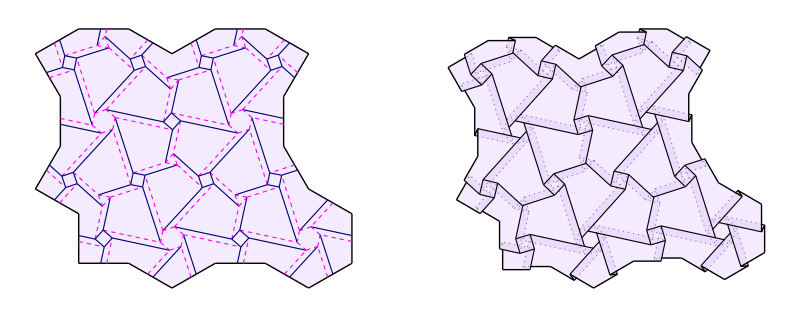

-Graphics-

#### Centered twists on two-colorable Archimedean tilings

A square lattice of identical tiles, based on a 2-coloring of the n=2 Archimedean tiling.

```mathematica
Module[{n,w,α,tpatch,types,patch,lattice,tiling,cliprect,ptiling},
n=2;
w=0.2;
α=30.°;
tpatch=TwoColorableArchimedeanPatch[n];
types={{M,M,M,M},{V,V,V,V}};
patch=UnitRegularPolygonCenteredTwistAltPatch[tpatch,w,α,types];
lattice=TwoColorableArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{-2,2},{0,3}];
cliprect=RectVertices[{.1,.1},{3.9,3.9}];
ptiling=PruneTiling[tiling,cliprect];
(* show tiling before and after pruning *)
Print[GraphicsRow[{
Graphics[{EmbedTiling[tiling,Tiling],PrunePoly[cliprect]}],Graphics[{EmbedTiling[ptiling,Tiling],PrunePoly[cliprect]}]}]/.TilingStyle[]];
(* crease pattern and folded form tilings *)
GraphicsRow[{
Graphics[EmbedTiling[ptiling,CreasePattern]],
Graphics[EmbedTiling[ptiling,FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

#### Offset twists on two-colorable Archimedean tilings

A square lattice of identical tiles, based on a 2-coloring of the n=2 Archimedean tiling.

```mathematica
Module[{n,w,d,tpatch,parity,types,patch,lattice,tiling,cliprect,ptiling},
n=2;
w=0.2;
d=0.1001;
tpatch=TwoColorableArchimedeanPatch[n];
parity=TwoColorableArchimedeanPatchParity[n];
types={{M,M,M,M},{M,M,M,M}};
patch=UnitRegularPolygonOffsetTwistPatch[tpatch,parity,w,d,types];
lattice=TwoColorableArchimedeanPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{-2,2},{0,3}];
cliprect=RectVertices[{.1,.1},{3.9,3.9}];
ptiling=PruneTiling[tiling,cliprect];
(* show tiling before and after pruning *)
Print[GraphicsRow[{
Graphics[{EmbedTiling[tiling,Tiling],PrunePoly[cliprect]}],Graphics[{EmbedTiling[ptiling,Tiling],PrunePoly[cliprect]}]}]/.TilingStyle[]];
(* crease pattern and folded form tilings *)
GraphicsRow[{
Graphics[EmbedTiling[ptiling,CreasePattern]],
Graphics[EmbedTiling[ptiling,FoldedForm2D]]}]/.OrigamiStyle[]
]//ShowExample
```

### 2-uniform tilings

#### Notes

There are twenty dstinct 2-uniform tilings of regular polygons. Here we create patches and lattice vectors for them all.

#### TwoUniformVertexTypes[n] TwoUniformName[n] TwoUniformPatch[n] TwoUniformPatchLatticeVectors[n]

TwoUniformVertexTypes[n] returns a list of the vertex types (used in constructing the name).

```mathematica
TwoUniformVertexTypes::badnum="TwoUniformVertexTypes[`1`] is not defined.";
```

```mathematica
TwoUniformVertexTypes[n_]:=(Message[TwoUniformVertexTypes::badnum,n];Abort[])
```

TwoUniformName[n] returns a string version of the name of the tiling, based on its vertex type.

```mathematica
TwoUniformName[n_]:=Module[{vnames},
vnames=StringJoin[Riffle[ToString/@#,"."]]&/@TwoUniformVertexTypes[n];
StringJoin["(",Riffle[ToString/@vnames,"; "],")"]]
```

TwoUniformPatch[n] returns the lattice patch for the tiling.

```mathematica
TwoUniformPatch::badnum="TwoUniformPatch[`1`] is not defined.";
```

```mathematica
TwoUniformPatch[n_]:=(Message[TwoUniformPatch::badnum,n];Abort[])
```

TwoUniversityPatchLatticeVectors[n] returns the lattice vectors for the tiling.

```mathematica
TwoUniversityPatchLatticeVectors::badnum="TwoUniversityPatchLatticeVectors[`1`] is not defined.";
```

```mathematica
TwoUniversityPatchLatticeVectors[n_]:=(Message[TwoUniversityPatchLatticeVectors::badnum,n];Abort[])
```

n=1: {{3,3,3,3,3,3},{3,3,3,3,6}}

```mathematica
TwoUniformVertexTypes[1]={{3,3,3,3,3,3},{3,3,3,3,6}};
```

```mathematica
TwoUniformPatch[1]=JoinTiling[{
{{UnitRegularPolygonTile,6}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,1,1}},(*4*)
{{UnitRegularPolygonTile,3},{4,2,1}},(*5*)
{{UnitRegularPolygonTile,3},{1,3,1}},(*6*)
{{UnitRegularPolygonTile,3},{6,1,1}},(*7*)
{{UnitRegularPolygonTile,3},{7,2,1}},(*8*)
{{UnitRegularPolygonTile,3},{8,1,1}},(*9*)
{{UnitRegularPolygonTile,3},{1,4,2}},(*10*)
{{UnitRegularPolygonTile,3},{10,2,1}},(*11*)
{{UnitRegularPolygonTile,3},{6,2,2}},(*12*)
{{UnitRegularPolygonTile,3},{12,2,1}},(*13*)
{{UnitRegularPolygonTile,3},{8,2,2}},(*14*)
{{UnitRegularPolygonTile,3},{14,2,1}},(*15*)
{{UnitRegularPolygonTile,3},{11,2,2}},(*16*)
{{UnitRegularPolygonTile,3},{16,2,1}},(*17*)
{{UnitRegularPolygonTile,3},{17,1,1}},(*18*)
{{UnitRegularPolygonTile,3},{18,2,1}},(*19*)
{{UnitRegularPolygonTile,3},{19,1,1}},(*20*)
{{UnitRegularPolygonTile,3},{20,2,1}}(*21*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[1]=PatchVectors[TwoUniformPatch[1],{1,1},{5,2},{16,3}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=1;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=2: {{3,3,3,3,3,3},{3,3,3,3,6}}

```mathematica
TwoUniformVertexTypes[2]={{3,3,3,3,3,3},{3,3,3,3,6}};
```

```mathematica
TwoUniformPatch[2]=JoinTiling[{
{{UnitRegularPolygonTile,6}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,1,1}},(*4*)
{{UnitRegularPolygonTile,3},{1,3,1}},(*5*)
{{UnitRegularPolygonTile,3},{5,1,1}},(*6*)
{{UnitRegularPolygonTile,3},{6,2,1}},(*7*)
{{UnitRegularPolygonTile,3},{1,4,2}},(*8*)
{{UnitRegularPolygonTile,3},{8,2,1}},(*9*)
{{UnitRegularPolygonTile,3},{9,1,1}},(*10*)
{{UnitRegularPolygonTile,3},{10,2,1}},(*11*)
{{UnitRegularPolygonTile,3},{11,1,1}},(*12*)
{{UnitRegularPolygonTile,3},{12,2,1}}(*13*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[2]=PatchVectors[TwoUniformPatch[2],{1,1},{4,2},{9,2}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=2;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=3: {{3,3,3,3,3,3},{3,3,3,4,4}}

```mathematica
TwoUniformVertexTypes[3]={{3,3,3,3,3,3},{3,3,3,4,4}};
```

```mathematica
TwoUniformPatch[3]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,1,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,1}},(*4*)
{{UnitRegularPolygonTile,3},{4,2,2}}(*5*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[3]=PatchVectors[TwoUniformPatch[3],{1,1},{4,2},{1,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=3;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=4: {{3,3,3,3,3,3},{3,3,3,4,4}}

```mathematica
TwoUniformVertexTypes[4]={{3,3,3,3,3,3},{3,3,3,4,4}};
```

```mathematica
TwoUniformPatch[4]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,2}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,1}},(*4*)
{{UnitRegularPolygonTile,3},{4,1,1}},(*5*)
{{UnitRegularPolygonTile,3},{5,2,1}},(*6*)
{{UnitRegularPolygonTile,3},{6,2,2}}(*7*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[4]=PatchVectors[TwoUniformPatch[4],{1,1},{6,2},{1,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=4;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=5: {{3,3,3,3,3,3},{3,3,4,12}}

```mathematica
TwoUniformVertexTypes[5]={{3,3,3,3,3,3},{3,3,4,12}};
```

```mathematica
TwoUniformPatch[5]=JoinTiling[{
{{UnitRegularPolygonTile,12}},(*1*)
{{UnitRegularPolygonTile,3},{1,3,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,1,1}},(*4*)
{{UnitRegularPolygonTile,4},{3,2,2}},(*5*)
{{UnitRegularPolygonTile,3},{5,3,2}},(*6*)
{{UnitRegularPolygonTile,3},{1,5,1}},(*7*)
{{UnitRegularPolygonTile,3},{7,2,2}},(*8*)
{{UnitRegularPolygonTile,4},{1,6,2}},(*9*)
{{UnitRegularPolygonTile,3},{9,4,2}},(*10*)
{{UnitRegularPolygonTile,3},{1,7,2}},(*11*)
{{UnitRegularPolygonTile,3},{11,3,2}},(*12*)
{{UnitRegularPolygonTile,4},{1,8,2}},(*13*)
{{UnitRegularPolygonTile,3},{13,4,3}},(*14*)
{{UnitRegularPolygonTile,3},{1,9,2}},(*15*)
{{UnitRegularPolygonTile,3},{14,3,2}}(*16*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[5]={PatchVector[TwoUniformPatch[5],{16,3},{9,3}],PatchVector[TwoUniformPatch[5],{1,1},{16,3}]}//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=5;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=6: {{3,3,3,3,3,3},{3,3,4,3,4}}

```mathematica
TwoUniformVertexTypes[6]={{3,3,3,3,3,3},{3,3,4,3,4}};
```

```mathematica
TwoUniformPatch[6]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,4},{2,2,2}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,1}},(*4*)
{{UnitRegularPolygonTile,3},{4,2,1}},(*5*)
{{UnitRegularPolygonTile,3},{5,1,1}},(*6*)
{{UnitRegularPolygonTile,4},{6,2,1}},(*7*)
{{UnitRegularPolygonTile,3},{7,1,1}},(*8*)
{{UnitRegularPolygonTile,3},{3,4,2}},(*9*)
{{UnitRegularPolygonTile,3},{1,3,2}},(*10*)
{{UnitRegularPolygonTile,3},{10,3,2}},(*11*)
{{UnitRegularPolygonTile,3},{3,3,2}},(*12*)
{{UnitRegularPolygonTile,4},{5,2,2}},(*13*)
{{UnitRegularPolygonTile,3},{7,3,2}},(*14*)
{{UnitRegularPolygonTile,3},{11,2,2}},(*15*)
{{UnitRegularPolygonTile,3},{15,2,1}},(*16*)
{{UnitRegularPolygonTile,3},{9,2,2}},(*17*)
{{UnitRegularPolygonTile,4},{12,3,2}},(*18*)
{{UnitRegularPolygonTile,3},{18,2,1}},(*19*)
{{UnitRegularPolygonTile,3},{13,3,2}},(*20*)
{{UnitRegularPolygonTile,3},{20,2,1}},(*21*)
{{UnitRegularPolygonTile,4},{14,2,2}}(*22*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[6]=PatchVectors[TwoUniformPatch[6],{1,1},{8,2},{15,3}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=6;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=7: {{3,3,3,3,3,3},{3,3,6,6}}

```mathematica
TwoUniformVertexTypes[7]={{3,3,3,3,3,3},{3,3,6,6}};
```

```mathematica
TwoUniformPatch[7]=JoinTiling[{
{{UnitRegularPolygonTile,3}},(*1*)
{{UnitRegularPolygonTile,6},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,1}},(*4*)
{{UnitRegularPolygonTile,3},{2,4,2}},(*5*)
{{UnitRegularPolygonTile,3},{5,2,1}},(*6*)
{{UnitRegularPolygonTile,6},{2,3,1}},(*7*)
{{UnitRegularPolygonTile,3},{7,3,1}}(*8*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[7]=PatchVectors[TwoUniformPatch[7],{1,1},{3,2},{5,3}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=7;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=8: {{3,3,3,3,6},{3,3,6,6}}

```mathematica
TwoUniformVertexTypes[8]={{3,3,3,3,6},{3,3,6,6}};
```

```mathematica
TwoUniformPatch[8]=JoinTiling[{
{{UnitRegularPolygonTile,6}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,2}},(*4*)
{{UnitRegularPolygonTile,3},{4,3,2}}(*5*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[8]=PatchVectors[TwoUniformPatch[8],{1,1},{3,2},{1,5}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=8;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=9: {{3,3,3,4,4},{3,3,4,3,4}}

```mathematica
TwoUniformVertexTypes[9]={{3,3,3,4,4},{3,3,4,3,4}};
```

```mathematica
TwoUniformPatch[9]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,1,1}},(*3*)
{{UnitRegularPolygonTile,4},{3,2,1}},(*4*)
{{UnitRegularPolygonTile,4},{4,2,1}},(*5*)
{{UnitRegularPolygonTile,3},{5,2,1}},(*6*)
{{UnitRegularPolygonTile,3},{1,4,3}},(*7*)
{{UnitRegularPolygonTile,4},{7,3,2}},(*8*)
{{UnitRegularPolygonTile,3},{8,2,1}},(*9*)
{{UnitRegularPolygonTile,3},{1,3,2}},(*10*)
{{UnitRegularPolygonTile,3},{10,2,1}},(*11*)
{{UnitRegularPolygonTile,4},{2,2,2}},(*12*)
{{UnitRegularPolygonTile,3},{12,2,1}},(*13*)
{{UnitRegularPolygonTile,3},{13,2,1}},(*14*)
{{UnitRegularPolygonTile,3},{5,3,2}},(*15*)
{{UnitRegularPolygonTile,3},{8,3,2}},(*16*)
{{UnitRegularPolygonTile,3},{16,2,2}},(*17*)
{{UnitRegularPolygonTile,4},{9,2,2}},(*18*)
{{UnitRegularPolygonTile,4},{18,2,1}},(*19*)
{{UnitRegularPolygonTile,3},{19,2,1}},(*20*)
{{UnitRegularPolygonTile,3},{12,3,2}},(*21*)
{{UnitRegularPolygonTile,4},{14,2,2}},(*22*)
{{UnitRegularPolygonTile,3},{17,3,2}},(*23*)
{{UnitRegularPolygonTile,4},{23,2,2}},(*24*)
{{UnitRegularPolygonTile,3},{18,3,2}},(*25*)
{{UnitRegularPolygonTile,3},{25,2,1}},(*26*)
{{UnitRegularPolygonTile,3},{19,3,2}},(*27*)
{{UnitRegularPolygonTile,4},{27,2,1}},(*28*)
{{UnitRegularPolygonTile,3},{20,2,2}},(*29*)
{{UnitRegularPolygonTile,4},{22,3,2}},(*30*)
{{UnitRegularPolygonTile,3},{24,3,2}},(*31*)
{{UnitRegularPolygonTile,4},{26,2,2}},(*32*)
{{UnitRegularPolygonTile,3},{32,2,1}},(*33*)
{{UnitRegularPolygonTile,3},{28,2,1}},(*34*)
{{UnitRegularPolygonTile,3},{30,3,2}},(*35*)
{{UnitRegularPolygonTile,3},{35,2,1}}(*36*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[9]=PatchVectors[TwoUniformPatch[9],{1,1},{6,2},{31,3}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=9;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=10: {{3,3,3,4,4},{3,3,4,3,4}}

```mathematica
TwoUniformVertexTypes[10]={{3,3,3,4,4},{3,3,4,3,4}};
```

```mathematica
TwoUniformPatch[10]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,4},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,1,1}},(*4*)
{{UnitRegularPolygonTile,3},{4,2,1}},(*5*)
{{UnitRegularPolygonTile,3},{5,1,1}},(*6*)
{{UnitRegularPolygonTile,3},{1,3,2}},(*7*)
{{UnitRegularPolygonTile,3},{7,2,1}},(*8*)
{{UnitRegularPolygonTile,3},{2,3,2}},(*9*)
{{UnitRegularPolygonTile,3},{9,2,1}},(*10*)
{{UnitRegularPolygonTile,4},{3,2,2}},(*11*)
{{UnitRegularPolygonTile,4},{5,2,2}}(*12*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[10]=PatchVectors[TwoUniformPatch[10],{1,1},{6,2},{7,3}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=10;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=11: {{3,3,4,3,4},{3,4,6,4}}

```mathematica
TwoUniformVertexTypes[11]={{3,3,4,3,4},{3,4,6,4}};
```

```mathematica
TwoUniformPatch[11]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,3},{1,4,3}},(*2*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*3*)
{{UnitRegularPolygonTile,4},{2,3,2}},(*4*)
{{UnitRegularPolygonTile,6},{1,3,2}},(*5*)
{{UnitRegularPolygonTile,4},{3,2,2}},(*6*)
{{UnitRegularPolygonTile,3},{6,2,1}},(*7*)
{{UnitRegularPolygonTile,3},{4,3,2}},(*8*)
{{UnitRegularPolygonTile,3},{6,3,2}},(*9*)
{{UnitRegularPolygonTile,4},{8,2,2}},(*10*)
{{UnitRegularPolygonTile,4},{5,3,1}},(*11*)
{{UnitRegularPolygonTile,3},{11,2,1}},(*12*)
{{UnitRegularPolygonTile,3},{10,3,2}},(*13*)
{{UnitRegularPolygonTile,4},{5,4,2}},(*14*)
{{UnitRegularPolygonTile,3},{11,3,2}}(*15*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[11]=PatchVectors[TwoUniformPatch[11],{2,1},{7,2},{14,3}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=11;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=12: {{3,3,4,4},{3,4,6,4}}

```mathematica
TwoUniformVertexTypes[12]={{3,3,3,4,4},{3,4,6,4}};
```

```mathematica
TwoUniformPatch[12]=JoinTiling[{
{{UnitRegularPolygonTile,6}},(*1*)
{{UnitRegularPolygonTile,4},{1,3,1}},(*2*)
{{UnitRegularPolygonTile,4},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,4},{1,4,2}},(*4*)
{{UnitRegularPolygonTile,3},{2,3,2}},(*5*)
{{UnitRegularPolygonTile,3},{5,2,2}},(*6*)
{{UnitRegularPolygonTile,3},{3,3,2}},(*7*)
{{UnitRegularPolygonTile,4},{4,3,2}},(*8*)
{{UnitRegularPolygonTile,3},{8,2,1}},(*9*)
{{UnitRegularPolygonTile,4},{9,2,2}},(*10*)
{{UnitRegularPolygonTile,4},{7,2,2}},(*11*)
{{UnitRegularPolygonTile,3},{10,3,2}},(*12*)
{{UnitRegularPolygonTile,3},{12,2,1}},(*13*)
{{UnitRegularPolygonTile,3},{11,3,2}},(*14*)
{{UnitRegularPolygonTile,3},{13,2,2}}(*15*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[12]=PatchVectors[TwoUniformPatch[12],{1,1},{3,2},{8,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=12;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=13: {{3,3,4,4},{4,4,4,4}}

```mathematica
TwoUniformVertexTypes[13]={{3,3,4,4},{4,4,4,4}};
```

```mathematica
TwoUniformPatch[13]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,4},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,2}}(*4*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[13]=PatchVectors[TwoUniformPatch[13],{1,1},{3,2},{1,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=13;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=14: {{3,3,4,4},{4,4,4,4}}

```mathematica
TwoUniformVertexTypes[14]={{3,3,4,4},{4,4,4,4}};
```

```mathematica
TwoUniformPatch[14]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,4},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,4},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,1}},(*4*)
{{UnitRegularPolygonTile,3},{4,2,2}}(*5*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[14]=PatchVectors[TwoUniformPatch[14],{1,1},{4,2},{1,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=14;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=15: {{3,3,4,4},{6,3,4,6,4}}

```mathematica
TwoUniformVertexTypes[15]={{3,3,4,4},{6,3,4,6,4}};
```

```mathematica
TwoUniformPatch[15]=JoinTiling[{
{{UnitRegularPolygonTile,6}},(*1*)
{{UnitRegularPolygonTile,4},{1,4,2}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,4},{1,3,1}},(*4*)
{{UnitRegularPolygonTile,4},{4,2,1}},(*5*)
{{UnitRegularPolygonTile,4},{5,2,1}},(*6*)
{{UnitRegularPolygonTile,4},{2,3,2}},(*7*)
{{UnitRegularPolygonTile,6},{3,2,1}},(*8*)
{{UnitRegularPolygonTile,3},{8,2,1}},(*9*)
{{UnitRegularPolygonTile,4},{7,3,2}},(*10*)
{{UnitRegularPolygonTile,3},{10,2,1}},(*11*)
{{UnitRegularPolygonTile,4},{11,2,2}},(*12*)
{{UnitRegularPolygonTile,4},{8,3,2}},(*13*)
{{UnitRegularPolygonTile,4},{9,2,2}},(*14*)
{{UnitRegularPolygonTile,3},{12,3,2}},(*15*)
{{UnitRegularPolygonTile,6},{13,3,2}},(*16*)
{{UnitRegularPolygonTile,3},{14,3,2}},(*17*)
{{UnitRegularPolygonTile,3},{16,4,2}}(*18*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[15]=PatchVectors[TwoUniformPatch[15],{1,1},{6,2},{10,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=15;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=16: {{3,3,6,6},{3,6,3,6}}

```mathematica
TwoUniformVertexTypes[16]={{3,3,6,6},{3,6,3,6}};
```

```mathematica
TwoUniformPatch[16]=JoinTiling[{
{{UnitRegularPolygonTile,6}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{1,3,2}}(*3*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[16]=PatchVectors[TwoUniformPatch[16],{1,1},{2,2},{1,5}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=16;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=17: {{3,4,3,12},{3,12,12}}

```mathematica
TwoUniformVertexTypes[17]={{3,4,3,12},{3,12,12}};
```

```mathematica
TwoUniformPatch[17]=JoinTiling[{
{{UnitRegularPolygonTile,12}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,4},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,3},{3,2,1}},(*4*)
{{UnitRegularPolygonTile,3},{1,3,1}},(*5*)
{{UnitRegularPolygonTile,3},{1,5,1}}(*6*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[17]=PatchVectors[TwoUniformPatch[17],{1,1},{4,2},{1,8}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=17;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=18: {{3,4,4,6},{3,6,3,6}}

```mathematica
TwoUniformVertexTypes[18]={{3,4,4,6},{3,6,3,6}};
```

```mathematica
TwoUniformPatch[18]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,6},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,4},{1,3,2}},(*3*)
{{UnitRegularPolygonTile,3},{2,5,2}},(*4*)
{{UnitRegularPolygonTile,3},{2,4,2}}(*5*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[18]=PatchVectors[TwoUniformPatch[18],{1,1},{2,3},{3,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=18;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=19: {{3,4,4,6},{3,6,3,6}}

```mathematica
TwoUniformVertexTypes[19]={{3,4,4,6},{3,6,3,6}};
```

```mathematica
TwoUniformPatch[19]=JoinTiling[{
{{UnitRegularPolygonTile,4}},(*1*)
{{UnitRegularPolygonTile,6},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,4},{1,3,2}},(*3*)
{{UnitRegularPolygonTile,3},{2,5,2}},(*4*)
{{UnitRegularPolygonTile,3},{2,4,2}},(*5*)
{{UnitRegularPolygonTile,4},{2,3,1}},(*6*)
{{UnitRegularPolygonTile,3},{6,2,1}},(*7*)
{{UnitRegularPolygonTile,4},{6,3,2}},(*8*)
{{UnitRegularPolygonTile,6},{7,2,2}},(*9*)
{{UnitRegularPolygonTile,3},{9,2,1}}(*10*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[19]=PatchVectors[TwoUniformPatch[19],{1,1},{10,2},{3,4}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=19;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=20: {{3,4,6,4},{4,6,12}}

```mathematica
TwoUniformVertexTypes[20]={{3,4,6,4},{4,6,12}};
```

```mathematica
TwoUniformPatch[20]=JoinTiling[{
{{UnitRegularPolygonTile,12}},(*1*)
{{UnitRegularPolygonTile,4},{1,4,1}},(*2*)
{{UnitRegularPolygonTile,3},{2,2,1}},(*3*)
{{UnitRegularPolygonTile,4},{3,2,2}},(*4*)
{{UnitRegularPolygonTile,6},{1,5,1}},(*5*)
{{UnitRegularPolygonTile,6},{1,7,2}},(*6*)
{{UnitRegularPolygonTile,4},{1,6,2}},(*7*)
{{UnitRegularPolygonTile,3},{7,3,2}},(*8*)
{{UnitRegularPolygonTile,4},{5,4,2}},(*9*)
{{UnitRegularPolygonTile,4},{8,3,2}},(*10*)
{{UnitRegularPolygonTile,6},{9,3,2}},(*11*)
{{UnitRegularPolygonTile,4},{11,3,1}}(*12*)
}]//FullSimplify;
```

```mathematica
TwoUniformPatchLatticeVectors[20]=PatchVectors[TwoUniformPatch[20],{1,1},{4,3},{6,5}]//FullSimplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,patch,lattice,tiling},
n=20;
Print["tiling = ",TwoUniformName[n]];
patch=TwoUniformPatch[n];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=TwoUniformPatchLatticeVectors[n];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

#### TwoColorableTwoUniform

These are the two-colorable 2-uniform tilings, for which both vertex types must be of even degree.

```mathematica
Module[{list},
list=Table[{n,TwoUniformVertexTypes[n]},{n,20}];
Select[list,And@@(EvenQ[Length[#]]&/@#⟦2⟧)&]//ColumnForm
]
```

{5,{{3,3,3,3,3,3},{3,3,4,12}}}
{7,{{3,3,3,3,3,3},{3,3,6,6}}}
{13,{{3,3,4,4},{4,4,4,4}}}
{14,{{3,3,4,4},{4,4,4,4}}}
{16,{{3,3,6,6},{3,6,3,6}}}
{18,{{3,4,4,6},{3,6,3,6}}}
{19,{{3,4,4,6},{3,6,3,6}}}

### Periodic equilateral pentagon tilings

#### Notes

There are five families of equilateral pentagons that tile the plane. Most of them are nonconvex, but there are five that are convex. Most of the five are neither cyclic (suitable for centered twists) or closed-back-twist (suitable for offset twist tilings), but if we subdivide a pentagon into a triangle and a quad, we can (sometimes) get a twist-tilable tiling.

This section constructs some of the pentagon tiles that tile periodically.

#### CairoPentagonAngles[δ] CairoSymmetricPentagonBaseAngle

CairoPentagonAngles[δ] returns the generic equilateral pentagon that tiles the plane using the Cairo tiling with first base angle δ.

Note that the tile with base angle π–δ is a rotated version of the mirror image tile.

```mathematica
CairoPentagonAngles[δ1_]:=CairoPentagonAngles[δ1]=Module[{angles,δ2,δ3},
angles=CompletePolygonAngles[{δ1,δ2,δ3,π-δ1}];
angles/.FindRoot[{1+Cos[δ1]-Cos[δ1-δ3]+Cos[δ1-δ2-δ3]-Cos[δ2+δ3],-Sin[δ1]+Sin[δ1-δ3]-Sin[δ1-δ2-δ3]-Sin[δ2+δ3]},{δ2,90°},{δ3,90°}]]
```

Example. the symmetric 90° tile.

```mathematica
Module[{angles},
angles=CairoPentagonAngles[90.°];
angles/°
]//ShowExample
```

CairoSymmetricPentagonBaseAngle returns the base angle for the other mirror-symmetric equilateral pentagon that tiles the plane using the Cairo tiling.

```mathematica
CairoSymmetricPentagonBaseAngle=Module[{angles,δ1,δ2,δ3},
angles=CompletePolygonAngles[{δ1,δ2,δ3,π-δ1}];
δ1/.FindRoot[{δ2-δ1,1+Cos[δ1]-Cos[δ1-δ3]+Cos[δ1-δ2-δ3]-Cos[δ2+δ3],-Sin[δ1]+Sin[δ1-δ3]-Sin[δ1-δ2-δ3]-Sin[δ2+δ3]},{δ1,90°},{δ2,90°},{δ3,90°}]];
```

In degrees.

```mathematica
CairoSymmetricPentagonBaseAngle/°//ShowExample
```

#### {UnitCairoPentagonTile, δ}

{UnitCairoPentagonTile, δ} is a tiletype that specifies a unit equilateral pentagon that supports a Cairo tiling, where δ is the base angle of the pentagon.

```mathematica
UnitCairoPentagonTile::usage="UnitCairoPentagonTile is a tile type that produces a unit equilateral pentagon that supports a Cairo tiling.";
```

There are two tiles that are mirror-symmetric. They have base angles of δ=90° and δ=CairoSymmetricPentagonBaseAngle (~ 98.7074°)

```mathematica
CairoSymmetricPentagonBaseAngle/°//ShowExample
```

#### RenderTile[{UnitCairoPentagonTile, δ}, decoration, opts]

RenderTile[{UnitCairoPentagonTile, δ}, decoration, opts] renders the tile as a PolygonTile for any decoration.

```mathematica
RenderTile[{UnitCairoPentagonTile,δ_},decoration_,opts___]:=Module[{angles,verts},
angles=CairoPentagonAngles[δ];
verts=UnitEquilateralPolygonVertices[angles];
RenderTile[{PolygonTile,verts},decoration,opts]]
```

Example

```mathematica
Module[{δ},
δ=CairoSymmetricPentagonBaseAngle;
Graphics[RenderTile[{UnitCairoPentagonTile,δ},Tiling]]/.TilingStyle[]
]//ShowExample
```

#### CairoPatch[δ]

CairoPatch[δ] returns a lattice patch of a periodic Cairo tiling using the Cairo pentagon with base angle δ. Note that the tiling is made up of both the tile and its mirror image, which we obtain by using a base angle of π-δ.

```mathematica
CairoPatch[δ_]:=JoinTiling[{
{{UnitCairoPentagonTile, δ}},
{{UnitCairoPentagonTile, π-δ},{1,4,4}},
{{UnitCairoPentagonTile, δ},{2,1,1}},
{{UnitCairoPentagonTile, π-δ},{3,4,4}}
}]//Chop;
```

Example: the taller skinny symmetric base angle.

```mathematica
Graphics[EmbedTiling[CairoPatch[CairoSymmetricPentagonBaseAngle],Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]//ShowExample
```

Example: 90°, the other angle that gives a mirror-symmetric tile.

```mathematica
CairoPatch[90.°]//ShowExample
```

```mathematica
Graphics[EmbedTiling[CairoPatch[90.°],Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]//ShowExample
```

#### CairoLatticeVectors[δ]

CairoLatticeVectors[δ] returns a pair of lattice vectors for a periodic Cairo tiling using the Cairo pentagon with base angle δ.

```mathematica
CairoLatticeVectors[δ_]:=PatchVectors[CairoPatch[δ],{4,5},{1,3},{3,2}]
```

Examples.

```mathematica
Module[{δ,patch,l1,l2,tiling},
δ=CairoSymmetricPentagonBaseAngle;
patch=CairoPatch[δ];
{l1,l2}=CairoLatticeVectors[δ];
tiling=MakeLatticeTiling[patch,{l1,l2},{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

```mathematica
Module[{δ,patch,l1,l2,tiling},
δ=90.°;
patch=CairoPatch[δ];
{l1,l2}=CairoLatticeVectors[δ];
tiling=MakeLatticeTiling[patch,{l1,l2},{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

Generic version.

```mathematica
Module[{δ,patch,l1,l2,tiling},
δ=105.°;
patch=CairoPatch[δ];
{l1,l2}=CairoLatticeVectors[δ];
tiling=MakeLatticeTiling[patch,{l1,l2},{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

#### DoubleCairoPatch[δ]

DoubleCairoPatch[δ] returns a lattice patch of a second form of the Cairo tiling that uses twice as many tiles. It’s basically a combination of the CairoPatch[δ] with its mirror image.

Note, though, that the double Cairo tiling reduces to the Cairo tiling for the two mirror-symmetric tiles, δ=90° and δ=CairoSymmetricPentagonBaseAngle.

```mathematica
DoubleCairoPatch[δ_]:=JoinTiling[{
{{UnitCairoPentagonTile, δ}},
{{UnitCairoPentagonTile, π-δ},{1,4,4}},
{{UnitCairoPentagonTile, δ},{2,1,1}},
{{UnitCairoPentagonTile, π-δ},{3,4,4}},
{{UnitCairoPentagonTile,π- δ},{2,5,2}},
{{UnitCairoPentagonTile, δ},{5,4,4}},
{{UnitCairoPentagonTile,  π-δ},{6,1,1}},
{{UnitCairoPentagonTile,δ},{3,1,1}}
}]//Chop;
```

Example

```mathematica
DoubleCairoPatch[90.°]
```

{{{UnitCairoPentagonTile,1.5708}},{{UnitCairoPentagonTile,1.5708},{-0.911438,2.41144},-1.5708,1.},{{UnitCairoPentagonTile,1.5708},{-0.911438,2.41144},-3.14159,1.},{{UnitCairoPentagonTile,1.5708},{0,0},1.5708,1.},{{UnitCairoPentagonTile,1.5708},{-0.911438,2.41144},0,1.},{{UnitCairoPentagonTile,1.5708},{-1.82288,4.82288},-1.5708,1.},{{UnitCairoPentagonTile,1.5708},{-1.82288,4.82288},-3.14159,1.},{{UnitCairoPentagonTile,1.5708},{-0.911438,2.41144},1.5708,1.}}

```mathematica
Graphics[EmbedTiling[DoubleCairoPatch[95.°],Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]//ShowExample
```

#### DoubleCairoLatticeVectors[δ]

DoubleCairoLatticeVectors[] returns a pair of lattice vectors for the double Cairo tiling based on a pentagon with base angle δ.

```mathematica
DoubleCairoLatticeVectors[δ_]:={PatchVector[DoubleCairoPatch[δ],{3,2},{1,3}],PatchVector[DoubleCairoPatch[δ],{4,5},{5,3}]}
```

Example

```mathematica
Module[{δ,patch,l1,l2,tiling},
δ=105.°;
patch=DoubleCairoPatch[δ];
{l1,l2}=DoubleCairoLatticeVectors[δ];
tiling=MakeLatticeTiling[patch,{l1,l2},{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

### Resch star tilings

#### Notes

In his patent 3,407,588, Ron Resch described a bunch of 3D structures that can be built upon certain classes of tilings of regular star polygons; they are those tilings in which every vertex contains exactly one star tip vertex and exactly one star reflex vertex for star polygons of order n=3 or higher. The possible tilings of that category are to be found in G&S, but not as a recognizable category, so I will call them “Resch star tilings.” They can be derived from k-uniform tilings, by recognizing that certain 2n-gons in the original tiling can be transformed into regular n-stars while preserving planarity of the tiling.

#### ReschStarName[n] ReschStarPatch[n, α] ReschStarPatchLatticeVectors[n, α]

```mathematica
ClearAll[ReschStarName,ReschStarPatch,ReschStarPatchLatticeVectors]
```

ReschStarName[n] returns a string giving the name of the nth ReschStar tiling.

```mathematica
ReschStarName::usage="ReschStarName[n] returns a string giving the name (vertex figure) of the nth ReschStar tiling with tip angle α.";
```

ReschStarPatch[n, α] returns a lattice patch for the nth Resch star tiling with tip angle α.

ReschStarPatchLatticeVectors[n, α] returns the corresponding lattice vectors for the nth Resch star tiling with tip angle α.

n=1 (derived from ArchimedeanName[9]):

```mathematica
ReschStarName[1]="((3.3_α)^*.3((.3)_α)^(**))";
```

```mathematica
ReschStarPatch[1,α_]:=ReschStarPatch[1,α]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularStarPolygonTile,3,α},{1,2,1}},
{{UnitRegularPolygonTile,3},{2,3,1}}
}]//Simplify;
```

```mathematica
ReschStarPatchLatticeVectors[1,α_]:=ReschStarPatchLatticeVectors[1,α]=PatchVectors[ReschStarPatch[1,α],{1,1},{2,2},{2,5}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,α,patch,lattice,tiling},
n=1;
α=40.°;
Print["tiling = ",ReschStarName[n]];
patch=ReschStarPatch[n,α];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ReschStarPatchLatticeVectors[n,α];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=2 (derived from TwoUniformName[16]):

```mathematica
ReschStarName[2]="(3.3((.3)_α)^*((.3)_α)^(**); (3.3_α)^*.3((.3)_α)^(**))";
```

```mathematica
ReschStarPatch[2,α_]:=ReschStarPatch[2,α]=JoinTiling[{
{{UnitRegularStarPolygonTile,3,α}},(*1*)
{{UnitRegularPolygonTile,3},{1,2,1}},(*2*)
{{UnitRegularPolygonTile,3},{1,3,2}},(*3*)
{{UnitRegularStarPolygonTile,3,α},{1,4,1}},(*4*)
{{UnitRegularPolygonTile,3},{4,1,1}},(*5*)
{{UnitRegularPolygonTile,3},{4,2,2}}(*6*)
}]//Simplify;
```

```mathematica
ReschStarPatchLatticeVectors[2,α_]:=ReschStarPatchLatticeVectors[2,α]=PatchVectors[ReschStarPatch[2,α],{1,1},{2,2},{4,4}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,α,patch,lattice,tiling},
n=2;
α=40.°;
Print["tiling = ",ReschStarName[n]];
patch=ReschStarPatch[n,α];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ReschStarPatchLatticeVectors[n,α];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=3 (derived from ArchimedeanName[3]):

Note that there is an equivalent tiling in which the hexagon is decomposed into six triangles.

```mathematica
ReschStarName[3]="((6.3_α)^*((.3)_α)^(**))";
```

```mathematica
ReschStarPatch[3,α_]:=ReschStarPatch[3,α]=JoinTiling[{
{{UnitRegularPolygonTile,6}},
{{UnitRegularStarPolygonTile,3,α},{1,2,6}},
{{UnitRegularStarPolygonTile,3,α},{1,3,6}}
}]//Simplify;
```

```mathematica
ReschStarPatchLatticeVectors[3,α_]:=ReschStarPatchLatticeVectors[3,α]=PatchVectors[ReschStarPatch[3,α],{1,1},{2,3},{3,4}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,α,patch,lattice,tiling},
n=3;
α=40.°;
Print["tiling = ",ReschStarName[n]];
patch=ReschStarPatch[n,α];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ReschStarPatchLatticeVectors[n,α];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=4 (derived from ArchimedeanName[12]):

```mathematica
ReschStarName[4]="((4.4_α)^*((.4)_α)^(**))";
```

```mathematica
ReschStarPatch[4,α_]:=ReschStarPatch[4,α]=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularStarPolygonTile,4,α},{1,2,8}}
}]//Simplify;
```

```mathematica
ReschStarPatchLatticeVectors[4,α_]:=ReschStarPatchLatticeVectors[4,α]=PatchVectors[ReschStarPatch[4,α],{1,1},{2,3},{2,6}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,α,patch,lattice,tiling},
n=4;
α=40.°;
Print["tiling = ",ReschStarName[n]];
patch=ReschStarPatch[n,α];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ReschStarPatchLatticeVectors[n,α];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

n=5 (derived from ArchimedeanName[10]):

```mathematica
ReschStarName[5]="((3.6_α)^*((.6)_α)^(**))";
```

```mathematica
ReschStarPatch[5,α_]:=ReschStarPatch[5,α]=JoinTiling[{
{{UnitRegularPolygonTile,3}},
{{UnitRegularStarPolygonTile,6,α},{1,2,12}},
{{UnitRegularPolygonTile,3},{2,5,1}}
}]//Simplify;
```

```mathematica
ReschStarPatchLatticeVectors[5,α_]:=ReschStarPatchLatticeVectors[5,α]=PatchVectors[ReschStarPatch[5,α],{1,1},{2,3},{2,8}]//Simplify;
```

Example. Show the name, patch, and a 2x2 lattice.

```mathematica
Module[{n,α,patch,lattice,tiling},
n=5;
α=40.°;
Print["tiling = ",ReschStarName[n]];
patch=ReschStarPatch[n,α];
Print[Graphics[EmbedTiling[patch,Tiling,TileVertexIndices->True,TileIndices->True],PlotLabel->"patch"]/.TilingStyle[]];
lattice=ReschStarPatchLatticeVectors[n,α];
tiling=MakeLatticeTiling[patch,lattice,{0,1},{0,1}];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True],PlotLabel->"tiling"]/.TilingStyle[]
]//ShowExample
```

## Nonperiodic tilings

#### Notes

Lots of interesting tilings are not periodic, but can still be defined and/or constructed efficiently as assemblies of smaller building blocks. In this section we set up functions to facilitate the construction of such tilings, along with some examples of specific tilings and families of tilings of interest.

### Combining patches

#### JoinTilingPatches[patchinfolist, opts] (options) Simplification, Numeric

JoinTilingPatches[patchinfolist, opts] takes a list of patches combined with offset information and assembles them into a tiling, i.e., a single list of tilespecs. The format of patchlist is
	{{patch_1, any}, {patch_2, {{h_2,i_2,j_2}, {k_2,l_2}}}, ...}
where patch_1 is an initial patch (a list of tilespecs), and each subsquent element is a pair consisting of a patch and an ordered list {{h_2,i_2,j_2}, {k_2,l_2}} that descriptions its position. In a fashion similar to JoinTiling, the (l-1)th and lth vertices of the kth tile in the patch is aligned with the (j+1)th and jth vertices (respectively) of the ith tile of the hth patch in the list (which must precede the current patch). Note that the variable any  after patch_1 is ignored and may be omitted. Options are:
	Simplify, Numeric have the same meaning as they do in JoinTiling.

```mathematica
JoinTilingPatches[patchinfolist_List,opts___]:=Module[{si,nm,sfn,np,patchlist,patchinfo,patch,h,i,j,k,l,sverts,tverts,ps,pr,po,nt,tilespec,tiletype,to,tr,ts,verts,pos},
si=Simplification/.{opts}/.Options[JoinTiling];
nm=Numeric/.{opts}/.Options[JoinTiling];
sfn=If[si===Automatic,If[nm,N,#&],Simplify];
np=Length[patchinfolist];
patchlist=First/@patchinfolist;(* just the patches *)
Do[(* for each patch *)
patchinfo=patchinfolist⟦ip⟧;
patch=patchinfo⟦1⟧;
{{h,i,j},{k,l}}=patchinfo⟦2⟧;
sverts=EmbedTile[patchlist⟦h,i⟧,TileVertices];(* source tile vertices *)
tverts=EmbedTile[patch⟦k⟧,TileVertices];(* target tile vertices within in this patch *)
(* scale, rotation, offset to be applied to each tile in the patch *)
{ps,pr,po}=ScaleRotationOffset[{tverts⟦l⟧,tverts⟦Mod[l-1,Length[tverts],1]⟧},{sverts⟦j⟧,sverts⟦Mod[j+1,Length[sverts],1]⟧}];
nt=Length[patch];
Do[ (* for each tile in patch, compose scale/rotation/offset *)
tilespec=patch⟦it⟧;
tiletype=tilespec⟦1⟧;
to=If[Length[tilespec]≥2,tilespec⟦2⟧,{0,0}];(* offset *)
tr=If[Length[tilespec]≥3,tilespec⟦3⟧,0];(* rotation *)
ts=If[Length[tilespec]≥4,tilespec⟦4⟧,1];(* scale *)
patchlist⟦ip,it⟧={tiletype,sfn[po+ps RotationMatrix2D[pr].to],sfn[pr+tr],sfn[ps*ts]}
,{it,nt}]
,{ip,2,np}];
Flatten[patchlist,1]]
```

Example.

```mathematica
Module[{patch1,patch2,patchinfolist,tiling},
patch1={{{UnitRegularPolygonTile,4}}};
patch2=JoinTiling[{
{{UnitRegularPolygonTile,4}},
{{UnitRegularPolygonTile,4},{1,2,1}},
{{UnitRegularPolygonTile,4},{2,3,1}}}];
Print[GraphicsRow[{
Graphics[EmbedTiling[patch1,Tiling,TileVertexIndices->True,TileIndices->True]],
Graphics[EmbedTiling[patch2,Tiling,TileVertexIndices->True,TileIndices->True]]}]/.TilingStyle[]];
patchinfolist={
{patch1,Null},
{patch2,{{1,1,2},{1,1}}},
{patch2,{{1,1,3},{1,1}}},
{patch2,{{1,1,4},{1,1}}},
{patch2,{{1,1,1},{1,1}}}
};
tiling=JoinTilingPatches[patchinfolist];
Graphics[EmbedTiling[tiling,Tiling,TileVertexIndices->True,TileIndices->True]]/.TilingStyle[]
]//ShowExample
```

### Goldberg central tessellations

#### Notes

We create patches for raw tilings, but not for twist patches. It is relatively straightforward to transforma a tiling patch into a twist tessellation patch using a substitution rule, and then you can pick up the oriented version of the tiling from the M/V assignment.

#### GoldbergPatch[m, n] GoldbergTiling[m, n, opts] (options) Simplification, Numeric

GoldbergPatch[m, n] returns a tiling patch of a Goldberg central tessellation with rotational order m and n rings, so it contains n^2 tiles. The first triangle is a unit triangle.

```mathematica
GoldbergPatch[m_,n_]:=Module[{ϕ},
ϕ=π/m;
Flatten[Table[{{{UnitTriangleTile,{2ϕ,π/2-ϕ,π/2-ϕ}},(i-1)U[0]+2Sin[ϕ](j-1)U[π/2+ϕ],0,1},If[i≠j,{{UnitTriangleTile,{π/2-ϕ,2ϕ,π/2-ϕ}},(i-1)U[0]+2Sin[ϕ](j-1)U[π/2+ϕ],2ϕ,1},Null]},{i,n},{j,i}],2]/.Null->Sequence[]]
```

Example

```mathematica
Module[{patch},
patch=GoldbergPatch[7,2];
Print["patch = ",ColumnForm[patch]];
Graphics[EmbedTiling[patch,Tiling,TileIndices->True,TileVertexIndices->True]]/.TilingStyle[]
]//ShowExample
```

GoldbergTiling[m, n] returns the full rotationally symmetric Goldberg tiling, i.e., m copies of the patch. Options are:
	Simplify, Numeric are passed through to JoinTilingPatches.

```mathematica
GoldbergTiling[m_,n_,opts___]:=Module[{patch},
patch=GoldbergPatch[m,n];
JoinTilingPatches[Table[{patch,{{i-1,1,3},{1,2}}},{i,m}],opts]]
```

Example

```mathematica
Module[{tiling},
tiling=GoldbergTiling[7,2,Numeric->True];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True,TileVertexIndices->True,Numeric->True]]/.TilingStyle[]
]//ShowExample
```

#### GoldbergOffsetTiling[m, n, o, opts]

GoldbergOffsetTiling[m, n, o, opts] returns an offset Goldberg tiling for even m where o specifies the relative offset of the bottom half of the tiling.

```mathematica
GoldbergOffsetTiling[m_, n_, o_, opts___]:=Module[{patch,top,bottom},
patch=GoldbergPatch[m,n];
top=JoinTilingPatches[Table[{patch,{{i-1,1,3},{1,2}}},{i,m/2}],opts];
bottom=top/.{{UnitTriangleTile,angles_},off_,rot_,s_}:>{{UnitTriangleTile,angles},RotationMatrix2D[π].off+{o,0},Mod[rot+π,2π,-π],s};
Join[top,bottom]]
```

Example

```mathematica
Module[{tiling},
tiling=GoldbergOffsetTiling[8,2,1,Numeric->True];
Graphics[EmbedTiling[tiling,Tiling,TileIndices->True,TileVertexIndices->True,Numeric->True]]/.TilingStyle[]
]//ShowExample
```

## Primal-dual twist tessellations

#### Notes

Primal-dual twist tessellations start with a plane graph, then construct the reciprocal diagram and use the two to create a tessellation for an arbitrary crease pattern, using the shrink-rotate algorithm used in Alex Bateman's Tess program.

#### {ρ, β} versus {γ, α}

A shrink-twist tessellation can be parameterized on two parameters: {ρ, β} where ρ is the shrinkage and β is the angle through which the shrunken polygon is rotated; or {γ, α} where γ is a parameter characteristic of the aspect ratio of the parallelograms, and α is the twist angle of the resulting twist. The utility of the second parameterization is that if {γ, α} produces a crease pattern, {γ, -α} produces the folded form.

### Primal-dual twist tessellation properties

#### Notes

This section defines functions for converting between the shrink-and-twist parameters (ρ,β) (shrink and twist of the primal graph), (ρρ,ββ) (shrink and twist of the dual graph), and (γ,α) (aspect ratio and twist angle for the tessellation).

#### ShrinkAndTwistParms[γ, α, opts] (options) TwistDirection, CW, CCW

ShrinkAndTwistParms[γ, α, opts] takes a desired parallelogram ratio γ, pleat angle α, and optional rotation direction, and  returns a list {ρ, β} the specifies the polygon dilation/shrinkage ρ and polygon rotation angle β that defines both the polygon and the parallelograms in the crease pattern and/or folded form. Options are:
	TwistDirection → CW | CCW, specifies the direction that the central polygon rotates going from the crease pattern to the folded form.

```mathematica
Options[ShrinkAndTwistParms]={
TwistDirection->CCW
};
```

```mathematica
ShrinkAndTwistParms[γ_,α_,opts___]:=Module[{dir,β,ρ},
dir=TwistDirection/.{opts}/.Options[ShrinkAndTwistParms];
ρ=γ/(√(1+γ^2+2 γ Sin[α]));
β=If[SameQ[dir,CCW],1,-1]ArcCos[(γ+Sin[α])/(√(1+γ^2+2 γ Sin[α]))];
{ρ,β}]
```

Examples

```mathematica
ShrinkAndTwistParms[0.5,15°,TwistDirection->CCW]//ShowExample
```

```mathematica
ShrinkAndTwistParms[0.5,-15°,TwistDirection->CCW]//ShowExample
```

```mathematica
ShrinkAndTwistParms[0.5,15°,TwistDirection->CW]//ShowExample
```

```mathematica
ShrinkAndTwistParms[0.5,-15°,TwistDirection->CW]//ShowExample
```

#### FoldedFormScaleRotation[γ, α] FoldedFormScale[γ, α] FoldedFormRotation[γ, α]

FoldedFormScaleRotation[γ, α] returns a pair {m, ϕ} that give proper scaling and rotational orientation to the computed folded form when we construct the folded form by reversing the sign of α. Specifically, if we construct a crease pattern for values (γ, α), then we can construct the properly scaled and rotated folded form by constructing the pattern for (γ, -α), then multiplying it by m and rotating it through an angle ϕ.

```mathematica
FoldedFormScaleRotation[γ_, α_]:=Module[{rcp,bcp,rff,bff},
{rcp,bcp}=ShrinkAndTwistParms[γ,α];
{rff,bff}=ShrinkAndTwistParms[γ,-α];
{rcp/rff,bcp-bff}
]
```

FoldedFormScale[γ, α] returns the factor by which the folded form pattern should be multipled to have the proper scale when computed from scale-and-rotate.

```mathematica
FoldedFormScale[γ_, α_]:=FoldedFormScaleRotation⟦1⟧
```

FoldedFormRotation[γ, α] returns the angle through which the folded form pattern should be rotated so that it matches the crease pattern.

```mathematica
FoldedFormRotation[γ_, α_]:=FoldedFormScaleRotation⟦2⟧
```

#### DualShrinkAndTwistParms[ρ, β]

DualShrinkAndTwistParms[ρ, β] returns the shrinkage and rotation parameters {ρρ, ββ} that apply to the dual faces.

```mathematica
DualShrinkAndTwistParms[ρ_,β_]:={√(1+ρ^2-2 ρ Cos[β]),-Sign[β]ArcCos[(1-ρ Cos[β])/(√(1+ρ^2-2 ρ Cos[β]))]}
```

### Primal-dual twist tessellation angle ranges [IN PROGRESS]

#### Notes

Whether a tessellation can be crease assigned depends on the pleat angle and the crease assignment. However, if the pleat angle is sufficiently small, it can always be crease assigned. Functions in this section evaluate this "safe" range of pleat angles.

#### PrimalDualUnsafeTwistAngleRange[pverts, pfaces, dverts, dfaces, bverts] (TBD: rewrite and use functions based on individual twist polygons, also use TObj’s)

PrimalDualUnsafeTwistAngleRange[pverts, pfaces, dverts, dfaces, bverts] take a primal graph with embedding pverts and faces pfaces, and the dual graph embedding dverts and dual faces dfaces, and a list of all the boundary vertex indices, and returns the range of angles {α_min,α_max} within which a crease assignment may not exist (depending on the twist assignment). That is, for pleat angles α *outside* this range, any crease assignment always works (at least locally) and the "standard" crease assignment for the pleat parallelgrams apply. Angle values are returned in radians.

```mathematica
PrimalDualUnsafeTwistAngleRange[pverts_,pfaces_,dverts_,dfaces_,bverts_]:=Module[{ptriples,dtriples,pangles,dangles,allangles},
ptriples=Take[#⟦1⟧,3]&/@(Select[Transpose[{pverts⟦#⟧,RotateLeft[pverts⟦#⟧],RotateLeft[pverts⟦#⟧,2],#}],!MemberQ[bverts,#⟦4⟧]&]&/@pfaces);dtriples=First[Transpose[{dverts⟦#⟧,RotateLeft[dverts⟦#⟧],RotateLeft[dverts⟦#⟧,2]}]&/@dfaces];
pangles=RotationAngle[#⟦2⟧-#⟦1⟧,#⟦3⟧-#⟦2⟧]&/@ptriples;
dangles=RotationAngle[#⟦2⟧-#⟦1⟧,#⟦3⟧-#⟦2⟧]&/@dtriples;
allangles=Join[pangles,dangles,π-pangles,π-dangles];
{Min[allangles],Max[allangles]}
]
```

Example

```mathematica
Module[{verts,edges,pverts,pedges,pfaces,dverts,dedges,dfaces,iverts,bverts,iedges,bedges,bfaces},
verts={{0,0},{1,0},{2,.5},{0,1},{1,1},{.5,2},{2,2}};
edges={{1,4},{1,2},{4,5},{2,5},{2,3},{3,7},{5,7},{4,6},{6,7}};
{pverts,pedges,pfaces,dverts,dedges,dfaces,iverts,bverts,iedges,bedges,bfaces}=AddTPrimalDualGraphTo[verts,edges];
dverts⟦1⟧={dverts⟦2,1⟧,dverts⟦3,2⟧};
Print[PrimalDualGraphics[pverts,pedges,dverts,dedges]];
PrimalDualUnsafeTwistAngleRange[pverts,pfaces,dverts,dfaces,bverts]/N[°]
]//ShowExample//Hold;
```

### Primal-dual twist tessellation construction

#### Notes

These functions take a TObj containing primal-dual graph data and turn that into a pair of edge-labeled plane graphs that correspond to the crease pattern and folded form.

#### ScaleAndTwistPoint[pt, ctr, ρ, β]

ScaleAndTwistPoint[pt, ctr, ρ, β] takes the point pt, scales it toward/away from ctr by a factor ρ, and rotates it about ctr through the CCW angle β.

```mathematica
ScaleAndTwistPoint[pt_,ctr_,ρ_,β_]:=ctr+ρ RotationMatrix2D[β].(pt-ctr)
```

Example

```mathematica
ScaleAndTwistPoint[{1,0},{-1,0},ρ,β]//ShowExample
```

#### MakePrimalDualTwistTessellationBoundaryEdge[bedge, bface, pverts, dverts, ρ, β]

MakePrimalDualBoundaryEdges[bedge, bface, pverts, dverts, ρ, β] takes a boundary edge bedge (specified as a vertex index pair) and the index bface of the dual vertex that corresponds to the face incident to that edge, an embedding of the primary vertices pverts, an embedding of the dual vertices dverts, a shrinkage parameter ρ, rotation angle β, and it returns a list {edgepair, edgetype} where edgepair is a vertex pair for the corresponding edge and edgetype is its type (which will always be B).

```mathematica
MakePrimalDualTwistTessellationBoundaryEdge[bedge_,bface_,pverts_,dverts_,ρ_,β_]:=Module[{p1,p2,d1,d2,p1d1,p1d2,p2d1,p2d2,p1b,p2b,s1,s2},
{p1,p2}=pverts⟦bedge⟧;
d1=dverts⟦bface⟧;
p1d1=ScaleAndTwistPoint[p1,d1,ρ,β];
p2d1=ScaleAndTwistPoint[p2,d1,ρ,β];
{{p1d1,p2d1},B}]
```

Example

```mathematica
Module[{γ,α,dir,ρ,β,pverts,pedges, pfaces,dverts,pefis,dfaces,iverts,bverts,bedge,bface,edgepair,edgetype},
γ=2.0;
α=20.°;
dir=CCW;
{ρ,β}=ShrinkAndTwistParms[γ,α,TwistDirection->dir];
Print["ρ=",ρ,", β=",β/°,"°"];
pverts={{0,0},{2,0},{4,0},{0,2},{2,2},{4,2},{0,4},{2,4},{4,4}};
pedges={{2,5},{4,5},{5,6},{5,8},{1,2},{2,3},{3,6},{6,9},{9,8},{8,7},{7,4},{4,1}};
pfaces={{1,2,5,4},{2,3,6,5},{4,5,8,7},{5,6,9,8}};
dverts={{1,1},{3,1},{1,3},{3,3}};
pefis={{1,2},{1,3},{2,4},{3,4},{1},{2},{2},{4},{4},{3},{3},{1}};
dfaces={{1,2,4,3}};
iverts={5};
bverts={1,2,3,6,9,8,7,4};
bedge=5;
bface=1;
{edgepair,edgetype}=MakePrimalDualTwistTessellationBoundaryEdge[pedges⟦bedge⟧,bface,pverts,dverts,ρ,β];
Show[GraphGraphics[MakeTGraph[pverts,pedges,pfaces]],Graphics[Style[Line[edgepair],edgetype]/.TypeToCreasePatternStyleRules]]/.OrigamiStyle[]
]//ShowExample
```

#### MakePrimalDualTwistTessellationInteriorEdges[iedge, dedge, pverts, dverts, bverts, ρ, β]

MakePrimalDualTwistTessellationInteriorEdges[iedge, dedge, pverts, dverts, bverts, ρ, β] takes an interior edge of the primal graph iedge (specified as a vertex index pair), its corresponding dual graph edge dedge, an embedding of the primary vertices pverts, an embedding of the dual vertices dverts, a list of the boundary vertex indices bverts, shrinkage parameter ρ, rotation angle β, and it returns lists {edgepairs, edgetypes} that specify the corresponding creases in the tessellation. edgepairs is a list of vertex pairs; edgetypes is a list of their types (M, V,  or B; U is not used).

In such a tessellation, the centers of rotation are the vertices of the dual graph; each interior edge transforms into a parallelogram; and each boundary edge transforms into a boundary edge of the tessellation. By suitable choice of the scale ρ and rotation angle β and the line specification linetype, this function can construct lines for either the CP or the FF.

```mathematica
MakePrimalDualTwistTessellationInteriorEdges[pedge_,dedge_,pverts_,dverts_,bverts_,ρ_,β_]:=Module[{p1,p2,d1,d2,p1d1,p1d2,p2d1,p2d2,p1b,p2b,ob,edgepairs,edgetypes},
{p1,p2}=pverts⟦pedge⟧;
{d1,d2}=dverts⟦dedge⟧;
p1d1=ScaleAndTwistPoint[p1,d1,ρ,β];
p2d1=ScaleAndTwistPoint[p2,d1,ρ,β];
p1d2=ScaleAndTwistPoint[p1,d2,ρ,β];
p2d2=ScaleAndTwistPoint[p2,d2,ρ,β];
p1b=MemberQ[bverts,pedge⟦1⟧];
p2b=MemberQ[bverts,pedge⟦2⟧];
ob=(p2d1-p1d1).(p1d2-p1d1)<0;(* p1d1 is obtuse *)
edgepairs={{p2d1,p1d1},{p1d1,p1d2},{p1d2,p2d2},{p2d1,p2d2}};
edgetypes={M,If[p1b,B,If[ob,M,V]],V,If[p2b,B,If[ob,V,M]]};
{edgepairs,edgetypes}]
```

Example

```mathematica
Module[{γ,α,dir,ρ,β,pverts,pedges, pfaces,dverts,dedges,dfaces,iverts,bverts,iedge,edgepairs,edgetypes},
γ=2.0;
α=20.°;
dir=CCW;
{ρ,β}=ShrinkAndTwistParms[γ,α,TwistDirection->dir];
Print["ρ=",ρ,", β=",β/°,"°"];
pverts={{0,0},{2,0},{4,0},{0,2},{2,2},{4,2},{0,4},{2,4},{4,4}};
pedges={{2,5},{4,5},{5,6},{5,8},{1,2},{2,3},{3,6},{6,9},{9,8},{8,7},{7,4},{4,1}};
pfaces={{1,2,5,4},{2,3,6,5},{4,5,8,7},{5,6,9,8}};
dverts={{1,1},{3,1},{1,3},{3,3}};
dedges={{1,2},{1,3},{2,4},{3,4}};
dfaces={{1,2,4,3}};
iverts={5};
bverts={1,2,3,6,9,8,7,4};
iedge=1;
{edgepairs,edgetypes}=MakePrimalDualTwistTessellationInteriorEdges[pedges⟦iedge⟧,dedges⟦iedge⟧,pverts,dverts,bverts,ρ,β];
Show[GraphGraphics[MakeTGraph[pverts,pedges,pfaces]],Graphics[{Style[DirectedEdgeLines[dverts,dedges],Blue],MapThread[Style[Line[#1],#2]&,{edgepairs,edgetypes}]/.TypeToCreasePatternStyleRules}]]/.OrigamiStyle[]
]//ShowExample
```

#### MakePrimalDualTwistTessellationEdges[tobj, γ, α, opts] (unchecked class) TPrimalDualGraph (options) PostRotation, TwistDirection

MakePrimalDualTwistTessellationEdges[tobj, γ, α, opts] takes a TPrimalDualGraph and constructs edge pairs and types that describes the tessellation pattern for the given tessellation. It returns a TGraph containing Vertices, Edges, and EdgeTypes (empty Faces) that describe the crease pattern or folded form. For positive α, you get the crease pattern; for negative α you get the folded form. Note that the order is fixed for a given primal-dual graph combination, so when we construct the edge pairs for both CP and FF, edges at the same position in the lists correspond. Options are:
	PostRotation→PrimalRotation | DualRotation | None, whether to rotate the result. Primal puts the primal polygons in their original rotation; Dual puts the dual polygons in their original rotation; None does neither.
	Direction→CCW | CW, which specifies the direction of the twist.

We take a full PrimalDualTPlaneGraph data as input, rather that building it up internally from a simpler structure like a TGraph. When you construct the TPrimalDualGraph, you can orient the DualEdges in order to choose the pleat directions (crease assignment) prior to feeding it to this routine.

```mathematica
PostRotation::usage="PostRotation is an option to makePrimalDualTwistTessellationEdges that specifies whether and how to rotate the resulting plane graph.";
```

```mathematica
PrimalRotation::usage="PrimalRotation is an option value for PostRotation that specifies to rotate the result so that the primal polygons are in their original orientation.";
```

```mathematica
DualRotation::usage="DualRotation is an option value for PostRotation that specifies to rotate the result so that the dual polygons are in their original orientation.";
```

```mathematica
Options[MakePrimalDualTwistTessellationEdges]={
PostRotation->None,
TwistDirection->CCW
};
```

```mathematica
MakePrimalDualTwistTessellationEdges[tobj_TObj,γ_,α_,opts___]:=Module[{pverts,pedges,dverts,dedges,iverts,bverts,iedges,bedges,bfaces,pr,edgepairs,edgetypes,ep,ty,ρ,β,ρρ,ββ,newverts,newedges},
{pverts,pedges,dverts,dedges,iverts,bverts,iedges,bedges,bfaces}=GetValues[tobj,{Vertices,Edges,DualVertices,DualEdges,InteriorVertices,BoundaryVertices,InteriorEdges,BoundaryEdges,BoundaryFaces}];
pr=PostRotation/.{opts}/.Options[MakePrimalDualTwistTessellationEdges];
{ρ,β}=ShrinkAndTwistParms[γ,α,opts];
{ρρ,ββ}=DualShrinkAndTwistParms[ρ,β];
edgepairs=edgetypes={};
MapThread[({ep,ty}=MakePrimalDualTwistTessellationInteriorEdges[#1,#2,pverts,dverts,bverts,ρ,β];JoinTo[edgepairs,ep];JoinTo[edgetypes,ty])&,{iedges,dedges}];
MapThread[({ep,ty}=MakePrimalDualTwistTessellationBoundaryEdge[#1,#2,pverts,dverts,ρ,β];AppendTo[edgepairs,ep];AppendTo[edgetypes,ty])&,{pedges⟦#⟧&/@bedges,bfaces}];
Switch[pr,
PrimalRotation,edgepairs=Map[RotationMatrix2D[-β].#&,edgepairs,{2}],
DualRotation,edgepairs=Map[RotationMatrix2D[-ββ].#&,edgepairs,{2}]];
{newverts,newedges}=Indexify[edgepairs,2];
MakeTGraph[newverts,newedges]//AddTAssignedTo[#,edgetypes]&]
```

Example. Note how the direction of the DualEdges sets the orientation of the pleats. (Also, that there’s no faces.)

```mathematica
Module[{γ,α,dir,ρ,β,pverts,pedges,tobj,tobjpdpg,tobjpdtte},
γ=2.0;
α=20.°;
dir=CCW;
{ρ,β}=ShrinkAndTwistParms[γ,α,TwistDirection->dir];
Print["ρ=",ρ,", β=",β/°,"°"];
pverts={{0,0},{2,0},{4,0},{0,2},{2,2},{4,2},{0,4},{2,4},{4,4}};
pedges={{2,5},{4,5},{5,6},{5,8},{1,2},{2,3},{3,6},{6,9},{9,8},{8,7},{7,4},{4,1}};
tobj=MakeTGraph[pverts,pedges]//AddTPlaneGraph;
tobjpdpg=AddTPrimalDualGraphTo[tobj];
tobjpdtte=MakePrimalDualTwistTessellationEdges[tobjpdpg,γ,α,PostRotation->PrimalRotation];
GraphicsRow[{
GraphGraphics[tobj],
PrimalDualGraphics[tobjpdpg,DualDirectedEdges->True],
CreasePatternGraphics[tobjpdtte]/.OrigamiStyle[]
}]
]//ShowExample
```

#### MakePrimalDualTwistTessellation[tobj, γ, α, opts] (check class) TPrimalDualGraph (options) PostRotation, TwistDirection

MakePrimalDualTwistTessellation[tobj, γ, α, opts] takes a TPrimalDualGraph and constructs the pair of plane graphs that describe both the crease pattern and folded form of a primal-dual tessellation. It returns a list {tobjcp, tobjff} of TAssignedPlaneGraphs, where tobjcp is the crease pattern plane graph, tobjff is the folded form plane graph. Options are:
	PostRotation→PrimalRotation | DualRotation | None, whether to rotate the result. Primal puts the primal polygons in their original rotation; Dual puts the dual polygons in their original rotation; None does neither.
	TwistDirection→CCW | CW, which specifies the direction of the twist.

Unlike other functions where we could compute the CP and FF independently, we have to compute them as a pair because we get the Faces of the FF from the embedded CP, since the embedding of the FF is not non-crossing.

Note that the choice of the FaceupFace for VisibleFoldedFormGraphics should be specified by you to ensure that the folded form display matches the crease directions of the crease pattern.

```mathematica
Options[MakePrimalDualTwistTessellation]={
PostRotation->None,
TwistDirection->CCW
};
```

```mathematica
MakePrimalDualTwistTessellation[tobj_TObj,γ_,α_,opts___]:=Module[{tobj1,vertsff},
AssertClass[tobj,TPrimalDualGraph,MakePrimalDualTwistTessellation];
tobj1=MakePrimalDualTwistTessellationEdges[tobj,γ,α,opts]//AddTPlaneGraphTo;
vertsff=GetValue[MakePrimalDualTwistTessellationEdges[tobj,γ,-α,opts],Vertices];
tobj1//AddTGraph2D[vertsff]]
```

Example. Primal-dual graph, the resulting twist crease pattern, and the folded form. Note that we must specify the FaceupFace.

```mathematica
Module[{γ,α,dir,ρ,β,pverts,pedges, tobjpd,tobjtt},
γ=2.0;
α=20.°;
dir=CCW;
{ρ,β}=ShrinkAndTwistParms[γ,α,TwistDirection->dir];
Print["CP: ρ=",ρ,", β=",β/°,"°"];
{ρ,β}=ShrinkAndTwistParms[γ,-α,TwistDirection->dir];
Print["FF: ρ=",ρ,", β=",β/°,"°"];
pverts={{0,0},{2,0},{4,0},{0,2},{2,2},{4,2},{0,4},{2,4},{4,4}};
pedges={{2,5},{4,5},{5,6},{5,8},{1,2},{2,3},{3,6},{6,9},{9,8},{8,7},{7,4},{4,1}};
tobjpd=MakeTGraph[pverts,pedges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo;
tobjtt=MakePrimalDualTwistTessellation[tobjpd,γ,α,TwistDirection->dir,PostRotation->PrimalRotation];
GraphicsRow[{
PrimalDualGraphics[tobjpd,DualDirectedEdges->True],
GraphGraphics[tobjtt],
CreasePatternGraphics[tobjtt],
VisibleFoldedFormGraphics[tobjtt,FaceupFace->3]}]/.OrigamiStyle[]
]//ShowExample
```

#### More examples of primal-dual twist tessellations

Example: a piece of a 3.4.6.4 tiling.

```mathematica
Module[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p19,p10,p11,p12,p13,p14,p15,p16,p17,p18,verts,edges,tobjpd,γ,α,dir,tobjtt},
p1={0,0};p2={1,0};p3=p2+U[60°];p4=p3+U[120°];p5=p4+U[180°];p6=p5+U[240°];
p7=p1+U[210°];p8=p1+U[270°];
p9=p2+U[270°];p10=p2+U[330°];
p11=p3+U[-30°];p12=p3+U[30°];
p13=p4+U[30°];p14=p4+U[90°];
p15=p5+U[90°];p16=p5+U[150°];
p17=p6+U[150°];p18=p6+U[210°];
verts={p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,7},{1,8},{2,9},{2,10},{3,11},{3,12},{4,13},{4,14},{5,15},{5,16},{6,17},{6,18},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,7}
};
tobjpd=MakeTGraph[verts,edges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo;
tobjpd=OrientEdgePairs[tobjpd,RadialAxialOrderingFn[(p1+p4/2),RadialMajor->True]];
γ=2.0;
α=30.°;
dir=CCW;
tobjtt=MakePrimalDualTwistTessellation[tobjpd,γ,α,TwistDirection->dir,PostRotation->PrimalRotation];
PartitionedGraphicsGrid[{
PrimalDualGraphics[tobjpd,DualDirectedEdges->True],
GraphGraphics[tobjtt],
CreasePatternGraphics[tobjtt],
VisibleFoldedFormGraphics[tobjtt,FaceupFace->1]},2]/.OrigamiStyle[]
]//ShowExample
```

Example of a primal-dual tessellation (3x3 square grid), oriented so that the central polygon is cyclic, and fully rendered.

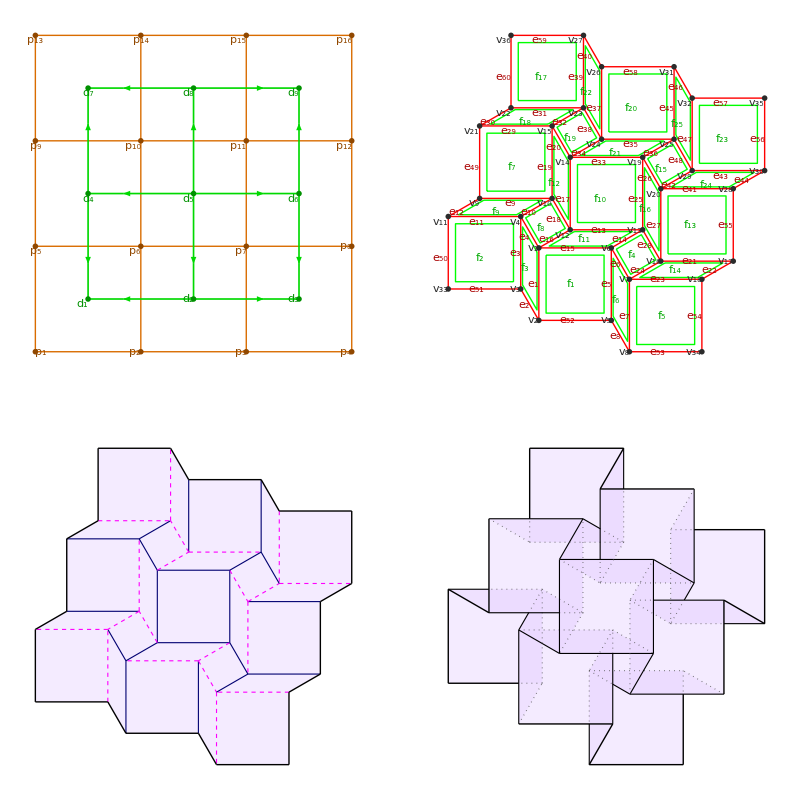

```mathematica
Module[{n,γ,α,dir,ρ,β,pverts,pedges, tobjpd,ctr,tobjtt},
n=3;
pverts=Flatten[Table[N[{i-1,j-1}],{j,n+1},{i,n+1}],1];
pedges=Join[Flatten[Table[{i+(n+1)(j-1),i+1+(n+1)(j-1)},{j,n+1},{i,n}],1],Flatten[Table[{i+(n+1)(j-1),i+(n+1)(j)},{j,n},{i,n+1}],1]];
tobjpd=MakeTGraph[pverts,pedges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo;
ctr=With[{dverts=GetValue[tobjpd,DualVertices]},Plus@@dverts/Length[dverts]];
tobjpd=OrientEdgePairs[tobjpd,RadialAxialOrderingFn[ctr]];
γ=2.0;
α=30.°;
dir=CCW;
tobjtt=MakePrimalDualTwistTessellation[tobjpd,γ,α,TwistDirection->dir,PostRotation->PrimalRotation];
PartitionedGraphicsGrid[{
PrimalDualGraphics[tobjpd,DualDirectedEdges->True],
GraphGraphics[tobjtt],
CreasePatternGraphics[tobjtt],
VisibleFoldedFormGraphics[tobjtt,FaceupFace->1]},2]/.OrigamiStyle[]
]
```

## More tilings for primal-dual tessellations

### Goldberg tilings

#### Notes

Michael Goldberg identified a family of radial isoceles triangle tilings in his 1955 paper "Central Tessellations." We create these tilings here. They're good for primal-dual tessellations.

The offset version of these tessellations gives a nonperiodic tiling that Alex Bateman has used for some of his tessellations.

#### GoldbergPoint[m, n, k, l]

GoldbergPoint[m, n, k, l] returns the coordinates of a point of a Goldberg radial isoceles triangle tiling that contains a unit edge from {0,0} to {1,0}, where m is the rotational order; n is the radial quantum number (0 is the origin); k indicates which wedge the point falls in; and l is the index of the point within that wedge. o is an offset value, which can be nonzero only for even m; it's used to create nonperiodic Goldberg tilings.

```mathematica
GoldbergPoint[m_,n_,k_,l_]:=Module[{ϕ},
ϕ=π/m;
RotationMatrix2D[2k ϕ].({n,0}+2l Sin[ϕ] U[π/2+ϕ])]
```

Example

```mathematica
Module[{m},
m=9;
Graphics[{
Style[Table[Point[GoldbergPoint[m,in,0,0]],{in,0,3}],Red,AbsolutePointSize[12]],
Style[Table[Point[GoldbergPoint[m,1,ik,0]],{ik,0,3}],Green,AbsolutePointSize[8]],
Style[Table[Point[GoldbergPoint[m,1,0,il]],{il,0,3}],Blue,AbsolutePointSize[4]]}]
]//ShowExample
```

#### MakeGoldbergTiling[m, n] MakeGoldbergTilingGraph[m, n] MakeGoldbergTilingPrimalDualGraph[m, n]

MakeGoldbergTiling[m, n] creates a list of point pairs that define line segments for a Goldberg tiling of rotational order m, radial order n, and horizontal offset o (which can be nonzero only for even values of m).

```mathematica
MakeGoldbergTiling[m_,n_]:=
Flatten[{
Table[{GoldbergPoint[m,in,ik,il],GoldbergPoint[m,in+1,ik,il]},{ik,0,m-1},{il,0,n},{in,il,n-1}],
Table[{GoldbergPoint[m,in,ik,il],GoldbergPoint[m,in,ik,il+1]},{ik,0,m-1},{il,0,n},{in,il+1,n}],
Table[{GoldbergPoint[m,in,ik,il],GoldbergPoint[m,in+1,ik,il+1]},{ik,0,m-1},{il,0,n},{in,il+1,n-1}]
},3]
```

Example

```mathematica
Module[{m,n,elist},
m=8;
n=2;
elist=MakeGoldbergTiling[m,n];
Graphics[Style[{Line[#],Point/@#}&/@elist,AbsolutePointSize[5],Orange],Frame->True]
]//ShowExample
```

MakeGoldbergTilingGraph[m, n] returns a TGraph representing a plane graph of a Goldberg tiling.

```mathematica
MakeGoldbergTilingGraph[m_,n_]:=Module[{elist,verts,edges},
elist=MakeGoldbergTiling[m,n]//N;
{verts,edges}=Indexify[elist,2];
MakeTGraph[verts,edges]]
```

Example

```mathematica
Module[{m,n,tobj},
m=9;
n=2;
tobj=MakeGoldbergTilingGraph[m,n];
GraphGraphics[tobj]
]//ShowExample
```

MakeGoldbergTilingPrimalDualGraph[m, n] returns a TPrimalDualGraph representing a primal-dual graph pair for a Goldberg tiling where the dual graph is a reciprocal diagram, and thus its vertices can be used as the centers of rotation for a shrink-rotate tessellation.

```mathematica
MakeGoldbergTilingPrimalDualGraph[m_,n_]:=Module[{tobj},
MakeGoldbergTilingGraph[m,n]//AddTPlaneGraphTo//AddTPrimalDualGraphTo//MakeTriangleGraphReciprocalDiagram]
```

Example

```mathematica
Module[{m,n,tobj},
m=9;
n=2;
tobj=MakeGoldbergTilingPrimalDualGraph[m,n];
PrimalDualGraphics[tobj]
]//ShowExample
```

That’s enough to make a complete tessellation. Typically you’d use an ordering function, like this example.

```mathematica
Module[{m,n,tobjpd,γ,α,dir,tobj},
m=7;
n=2;
tobjpd=MakeGoldbergTilingPrimalDualGraph[m,n];
tobjpd=OrientEdgePairs[tobjpd,RadialAxialOrderingFn[{0,0}]];
γ=1.15;
α=25.71°;
dir=CW;
tobj=MakePrimalDualTwistTessellation[tobjpd,γ,α,TwistDirection->dir,PostRotation->PrimalRotation];
GraphicsRow[{
PrimalDualGraphics[tobjpd,DualDirectedEdges->True],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->1]}]/.OrigamiStyle[]
]//ShowExample
```

#### MakeOffsetGoldbergTiling[m, n, o] MakeOffsetGoldbergTilingGraph[m, n, o] MakeOffsetGoldbergTilingPrimalDualGraph[m, n, o]

MakeOffsetGoldbergTiling[m, n, o] returns a list of point pairs for a Goldberg tiling whose top and bottom halves are offset by o units relative to one another (but the overall pattern is still centered on the origin). Rotational order m must be even or an error will result.

```mathematica
MakeOffsetGoldbergTiling::badrot="The rotational order `1` must be even.";
MakeOffsetGoldbergTiling::badoff="The offset `1` must be positive.";
```

```mathematica
MakeOffsetGoldbergTiling[m_,n_,o_:1]:=Module[{elist,etop,ebot},
If[Mod[m,2]≠0,Message[MakeOffsetGoldbergTiling::badrot,m];Abort[]];
If[o<0,Message[MakeOffsetGoldbergTiling::badoff,o];Abort[]];
elist=MakeGoldbergTiling[m,n];
{etop,ebot}=GatherBy[elist,N[#⟦1,2⟧]<-10^-6||N[#⟦2,2⟧]<-10^-6&];
Join[Map[{-o/2,0}+#&,etop,{2}],Map[{o/2,0}+#&,ebot,{2}],Table[{{n+io-o/2,0},{n+io+1-o/2,0}},{io,0,o-1}]]]
```

```mathematica
Module[{m,n,elist},
m=8;
n=2;
elist=MakeOffsetGoldbergTiling[m,n,1];
Graphics[Style[{Line[#],Point/@#}&/@elist,AbsolutePointSize[5],Orange],Frame->True]
]//ShowExample
```

MakeOffsetGoldbergTilingGraph[m, n, o] returns a TGraph representing a plane graph of an offset Goldberg tiling.

```mathematica
MakeOffsetGoldbergTilingGraph[m_,n_,o_:1]:=Module[{elist,verts,edges},
elist=MakeOffsetGoldbergTiling[m,n,o]//N;
{verts,edges}=Indexify[elist,2];
MakeTGraph[verts,edges]]
```

Example

```mathematica
Module[{m,n,tobj},
m=8;
n=2;
tobj=MakeOffsetGoldbergTilingGraph[m,n,1];
GraphGraphics[tobj]
]//ShowExample
```

MakeOffsetGoldbergTilingPrimalDualGraph[m, n, o] returns a TPrimalDualGraph representing a primal-dual graph pair for an offset Goldberg tiling. As above, the DualVertices are chosen to make the dual graph a reciprocal diagram, and thus the shrink-rotate algorithm will produce a valid tessellation.

```mathematica
MakeOffsetGoldbergTilingPrimalDualGraph[m_,n_,o_:1]:=Module[{tobj},
tobj=MakeOffsetGoldbergTilingGraph[m,n]//AddTPlaneGraphTo//AddTPrimalDualGraphTo//MakeTriangleGraphReciprocalDiagram]
```

Example

```mathematica
Module[{m,n,tobj},
m=8;
n=1;
tobj=MakeOffsetGoldbergTilingPrimalDualGraph[m,n,1];
PrimalDualGraphics[tobj]
]//ShowExample
```

#### Example of an offset Goldberg tiling tessellation

```mathematica
Module[{
m,n,o,tobjpd,γ,α,tobj},
m=8;
n=2;
o=1;
tobjpd=MakeOffsetGoldbergTilingPrimalDualGraph[m,n,o];
tobjpd=OrientEdgePairs[tobjpd,RadialAxialOrderingFn[{0,0},RadialMajor->False]];
γ=1.0;
α=22.0°;
tobj=MakePrimalDualTwistTessellation[tobjpd,γ,α];
GraphicsRow[{
PrimalDualGraphics[tobjpd,DualDirectedEdges->True],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->-1]
}]/.OrigamiStyle[]
]//ShowExample
```

### Voronoi/Delaunay tilings

#### Notes

Voronoi-Delaunay tessellations are a special case of primal-dual tessellations, which make use of the nice fact that the Delaunay Triangulation of a set of points and the Voronoi Diagram are reciprocal diagrams of one another. So, given a set of points, once can construct a tessellation from that set by constructing  the DT or VD, without having to solve a LP problem for the reciprocal diagram.

This uses the ComputationalGeometry package, which we already read in as part of our plane graph functions.

#### MakeDelaunayTriangulationPrimalDualGraph[points]

MakeDelaunayTriangulationPrimalDualGraph[points] takes a list of points points, constructs the Delaunay triangulation of those points, and then turns that triangulation into a primal-dual pair where the dual is the reciprocal diagram for the primal graph. It returns a TPrimalDualGraph. The convex hull of the set of points will be the boundary of the primal graph.

The orthogonal interior dual will be a Voronoi diagram of the interior points of the set (those points not on the convex hull), but since this is a triangle graph, we can compute the dual graph from the circumcenters of all the triangles, using our MakeTriangleGraphReciprocalDiagram function.

```mathematica
MakeDelaunayTriangulationPrimalDualGraph[pverts_]:=Module[{delval,pedges,tobj,pfaces,dverts,dedges,dfaces,iverts,bverts,iedges,bedges,bfaces},
delval=DelaunayTriangulation[pverts];
pedges=Union[Flatten[Transpose[{Table[#⟦1⟧,{Length[#⟦2⟧]}],#⟦2⟧}]&/@delval,1],SameTest->SameEdgeQ];
MakeTGraph[pverts,pedges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo//MakeTriangleGraphReciprocalDiagram]
```

Example

```mathematica
Module[{pverts,tobjpd,γ,α,dir,tobj},
SeedRandom[0];
pverts=Table[0.1+0.8 {Random[],Random[]},{8}]; 
tobjpd=MakeDelaunayTriangulationPrimalDualGraph[pverts];
γ=1.0;
α=15.°;
dir=CCW;
tobj=MakePrimalDualTwistTessellation[tobjpd,γ,α,Direction->dir];
GraphicsRow[{
Graphics[PrimalDualGraphics[tobjpd,DualDirectedEdges->True]⟦1⟧,Frame->True],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->-1]
}]/.OrigamiStyle[]
]//ShowExample
```

#### MakeBoundedVoronoiDiagramPrimalDualGraph[bounds, points]

MakeBoundedVoronoiDiagramPrimalDualGraph[bounds, points] takes a list of points bounds, which is a bounding polygon, and a list of contained points points, and constructs the bounded Voronoi diagram; this becomes the primal graph. It returns a TPrimalDualGraph. The Delaunay triangulation of points will be the dual graph. It returns the list of plane graph data needed to construct a primal-dual tessellation.

In general, Voronoi diagrams tend to have long protruding spikes, so if we used an unbounded Voronoi diagram, the primal graph would be spiky as well. By supplying a boundary, we effectively "cut off" those spikes, producing a more well-behaved (and therefore aesthetic) primal graph.

Since we use the built-in function BoundedDiagram to compute the bounded Voronoi diagram, the boundary vertices must lie within unique Voronoi cells. That means you should use relatively simple boundaries; if you use a point-dense boundary (like a polygonal approximation to a circle) you will likely have more than one boundary point in a Voronoi cell and the algorithm will fail and Abort.

```mathematica
MakeBoundedVoronoiDiagramPrimalDualGraph::notuniq="MakeBoundedVoronoiDiagramPrimalDualGraph failed because BoundedDiagram failed (see preceding message for details).";
```

```mathematica
MakeBoundedVoronoiDiagramPrimalDualGraph[bounds_,points_]:=Module[{delval,bd,vorverts,vadj,pverts,pfaces1,pedges,dverts1,pfaces,dverts,tobj},
(* construct the Delaunay triangulation and the Voronoi diagram of the points *)
delval=DelaunayTriangulation[points];
bd=BoundedDiagram[bounds,points,delval];
If[SameQ[Head[bd],BoundedDiagram],Message[MakeBoundedVoronoiDiagramPrimalDualGraph::notuniq];Abort[]];
{vorverts,vadj}=bd;
(* construct verts and edges; also note the faces and dual vertices for later use *)
pverts=vorverts;
pfaces1=Last/@vadj;
pedges=Union[Flatten[Transpose[{#,RotateLeft[#]}]&/@pfaces1,1],SameTest->SameEdgeQ];
dverts1=points;
(* build all the plane graph data. Note that pfaces will in general be a different order than pfaces1. *)
tobj=MakeTGraph[pverts,pedges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo;
(* now we replace the (approximate) dual vertices with the real ones, using the permutation derived from  face lists. *)
{pfaces,dverts}=GetValues[tobj,{Faces,DualVertices}];
Do[If[SameFaceQ[pfaces⟦i⟧,pfaces1⟦j⟧],dverts⟦i⟧=dverts1⟦j⟧],{i,Length[pfaces]},{j,Length[pfaces]}];
ReplacePropertyIn[tobj,DualVertices->dverts]]
```

Example

```mathematica
Module[{bounds,points,tobjpd,γ,α,dir,tobj},
bounds={{0,0},{1,0},{1,1},{0,1}};
SeedRandom[0];
points=Table[0.1+0.8 {Random[],Random[]},{8}]; (* Use 7 pts to test the error, use 8 for complete function *)
tobjpd=MakeBoundedVoronoiDiagramPrimalDualGraph[bounds,points];
γ=1.0;
α=15.°;
dir=CCW;
tobj=MakePrimalDualTwistTessellation[tobjpd,γ,α,Direction->dir];
GraphicsRow[{
PrimalDualGraphics[tobjpd],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->-1]
}]/.OrigamiStyle[]
]//ShowExample
```

### Penrose rhomb tilings

#### Notes

Penrose rhomb tilings lend themselves to primal-dual tessellations because they possess a reciprocal diagram whose vertices can be readily calculated. Penrose rhomb tilings can be constructed by an operation called deflation that acts on triangles, pairs of which make the rhombs. When you deflate an initial set, you will typically be left with some half-rhombs on the border of the pattern. In our case, we will keep those triangles (which have their own dual vertices) so that the resulting tiling has a smooth border. You can, if you like, prune them away.

#### MakePenroseRhombTilingPrimalDualGraph[n, opts] (options) PenroseBorderTriangles

MakePenroseRhombTilingPrimalDualGraph[n, opts] returns the plane graph data describing a Penrose rhomb tiling that is created by deflating either a Sun or Star (thereby always giving a rhomb, rather than a kite-dart, tiling). n=0 starts with a Star; n=1 starts with a Sun. Options are:
	BorderTriangles→True | False, specifies whether to include half-rhombs on the border (gives a smoother outline).

```mathematica
PenroseBorderTriangles::usage="PenroseBorderTriangles is an option to MakePenroseRhombTilingPrimalDualGraph that specifies whether to include half-rhombs on the border of the pattern.";
```

```mathematica
Options[MakePenroseRhombTilingPrimalDualGraph]={
PenroseBorderTriangles->True
};
```

```mathematica
MakePenroseRhombTilingPrimalDualGraph[n_,opts___]:=Module[{bt,sd,ϕ,a1,a2,o1,o2,deflate,tl,tdv,dv,cmp,pairs,solos,lut,pverts,pedges,tobj,pfaces,dverts},
bt=PenroseBorderTriangles/.{opts}/.Options[MakePenroseRhombTilingPrimalDualGraph];
(* infrastructure for building Penrose tilings *)
ϕ=GoldenRatio//N;
sd=Switch[Mod[n,2],
1,Module[{i},Flatten[Table[{a1[{Cos[72 i °],Sin[72 i  °]},{0,0},{Cos[(36+72 i)  °],Sin[(36+72 i)  °]}],a1[{Cos[72 i  °],Sin[72 i  °]},{0,0},{Cos[(-36+72 i)  °],Sin[(-36+72 i)  °]}]},{i,0,4}]]],
0,Module[{i},Flatten[Table[{o1[{0,0},{Cos[72 i  °],Sin[72 i  °]},ϕ {Cos[(36+72 i)  °],Sin[(36+72 i)  °]}],o1[{0,0},{Cos[72 i  °],Sin[72 i  °]},ϕ {Cos[(-36+72 i)  °],Sin[(-36+72 i)  °]}]},{i,0,4}]]],
_,Message[MakePenroseRhombTilingPrimalDualGraph::badopt,sd];Abort[]]//N;
(* deflation rules *)
deflate[a1[x_,y_,z_]]:=With[{d=((ϕ-1) x+(2-ϕ) y)},{a2[d,z,x],o2[z,d,y]}];
deflate[o1[x_,y_,z_]]:={o2[x,y,z]};
deflate[a2[x_,y_,z_]]:={a1[x,y,z]};
deflate[o2[x_,y_,z_]]:=With[{d=(2-ϕ) x+(ϕ-1) z},{o1[z,d,y],a1[y,x,d]}];
deflate[x_List]:=Join@@(deflate/@x);
deflate[x_List,0]:=x;
deflate[x_List,nn_]:=Nest[deflate,x,nn];
(* the desired raw tiling in triangle form *)
tl=deflate[sd,2⌊n/2⌋+1];
(* record the dual vertex coordinates for each triangle *)
tdv=tl/.{a2[x_,y_,z_]:>x+(1/2-ϕ/2)(z-x),o2[x_,y_,z_]:>z+(1-ϕ/2)(x-z)};
(* indexify all vertex coordinates *)
{pverts,tl}=Indexify[tl,2];
(* group triangles into pairs and isolated triangles (which are on the border) *)
cmp[a2[x1_,y1_,z1_], a2[x2_,y2_,z2_]]:=(x1==x2)&&(z1==z2);
cmp[o2[x1_,y1_,z1_], o2[x2_,y2_,z2_]]:=(x1==x2)&&(z1==z2);
pairs={};
solos={};
Do[If[cmp[tl⟦i⟧,tl⟦j⟧],AppendTo[pairs,tl⟦i⟧];AppendTo[pairs,tl⟦j⟧]],{i,2,Length[tl]},{j,i-1}];
Do[If[!IntersectsQ[{tl⟦i⟧},pairs],AppendTo[solos,tl⟦i⟧]],{i,Length[tl]}];
(* build edges of rhombs and border triangles *)
pedges=Flatten[pairs/.{a2[x_,y_,z_]|o2[x_,y_,z_]:>{{x,y},{y,z}}},1]~Join~Flatten[solos/.{a2[x_,y_,z_]|o2[x_,y_,z_]:>{{x,y},{y,z},{z,x}}},1];
pedges=Union[Sort/@pedges];
(* build the full set of plane graph data, using centroids for the dual vertices *)
tobj=MakeTGraph[pverts,pedges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo;
pfaces=GetValue[tobj,Faces];
(* but substitute the dual vertices we already computed *)
{dv,tdv}=Indexify[tdv];
(* lut is a lookup table that maps a trio of pvert indices to an index into dv *)
lut=Transpose[{List@@#&/@tl,tdv}];
dverts=dv⟦Table[Select[lut,IntersectsQ[pfaces⟦i⟧,{#⟦1,1⟧}]&&IntersectsQ[pfaces⟦i⟧,{#⟦1,2⟧}]&&IntersectsQ[pfaces⟦i⟧,{#⟦1,3⟧}]&]⟦1,2⟧,{i,Length[pfaces]}]⟧;
ReplacePropertyIn[tobj,DualVertices->dverts]]
```

Example

```mathematica
Module[{tobjpd,γ,α,dir,tobj},
tobjpd=MakePenroseRhombTilingPrimalDualGraph[3];
γ=1;
α=15.°;
dir=CCW;
tobj=MakePrimalDualTwistTessellation[tobjpd,γ,α,Direction->dir];
GraphicsRow[{
PrimalDualGraphics[tobjpd],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->-1]
}]/.OrigamiStyle[]
]//ShowExample
```

### Rotational trapezoid tilings

#### Notes

For a pattern composed of trapezoids and triangles, the trapezoids are circumscribable; the triangles are, too; so we’re guaranteed to have a primal-dual twist tessellation. So we can build a rotationally symmetric graph of trapezoids and use it for a tessellation.

#### MakeRotationalTrapezoidPrimalDualGraph[m, rvals, opts] (options) IncludeCenter

MakeRotationalTrapezoidPrimalDualGraph[m, rvals, opts] constructs a TPrimalDualGraph where the primal graph is a rotational trapezoid graph and the dual is its reciprocal diagram. The rotational order is m. rvals is a list of radial values of strictly increasing magnitude that define the radial spacing from the center. Options are:
	IncludeCenter → True | False, which specifies whether to include the center point in the primal graph.

```mathematica
Options[MakeRotationalTrapezoidPrimalDualGraph]={
IncludeCenter->False
};
```

```mathematica
MakeRotationalTrapezoidPrimalDualGraph[m_, rvals_, opts___]:=Module[{ic,vfn,tobj,verts,faces,dverts},
ic=IncludeCenter/.{opts}/.Options[MakeRotationalTrapezoidPrimalDualGraph];
vfn[i_,j_]:=If[i==0,{0,0},rvals⟦i⟧U[2π (j-1)/m]];
Off[N::meprec];(* to prevent annoying and unimportant warning *)
tobj=MakeRotationalMesh[Length[rvals],m,vfn,IncludeCenter->ic]//AddTPlaneGraph//AddTPrimalDualGraph;
(* tweak dual vertices to be the circumcenters of their respective faces *)
{verts,faces}=GetValues[tobj,{Vertices,Faces}];
dverts=Circumcenter/@N[verts⟦#⟧&/@faces];
On[N::meprec];
tobj//ReplaceProperty[DualVertices->dverts]
]
```

Example.

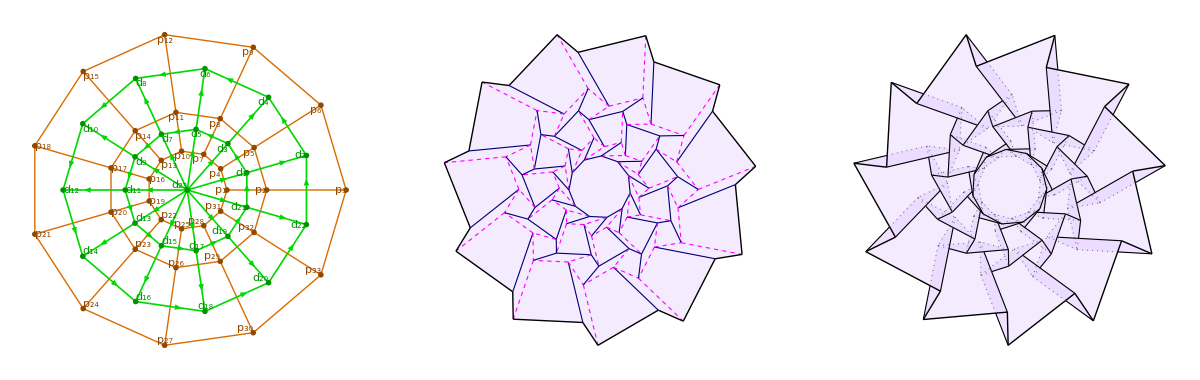

```mathematica
Module[{m,rvals,tobjpd,fn,γ,α,dir,tobj},
m=11;
rvals={1,2,4};
tobjpd=MakeRotationalTrapezoidPrimalDualGraph[m,rvals,IncludeCenter->False];
fn=RadialAxialOrderingFn[{0,0},RadialMajor->True];
tobjpd=OrientEdgePairs[tobjpd,fn];
γ=2;
α=20.°;
dir=CW;
tobj=MakePrimalDualTwistTessellation[tobjpd,γ,α,Direction->dir];
GraphicsRow[{
PrimalDualGraphics[tobjpd,DualDirectedEdges->True],
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj,FaceupFace->1]
}]/.OrigamiStyle[]
]
```

## Primal-dual flagstone tessellations

#### Notes

Flagstone tessellations take a primal-dual graph pair and construct a crease pattern by shrinking the primal polygons and adding double pleats in the “grout” regions between the shrunken polygons, and then tries make all the pleats play nicely where they come together at the vertices. This algorithm strives for maximally balanced pleats and chooses the centroid of the grout polygon as the alignment point for each central polygon.

### Primal-dual flagstone tessellations

#### MakePrimalDualFlagstoneTessellation[tobj, ρ, opts] (checked class) TPrimalDualGraph (options) GroupFaces

MakePrimalDualFlagstoneTessellation[tobj, ρ] take a TPrimalDualGraph and constructs the crease pattern and folded form of a primal-dual flagstone tessellation using a shrinkage factor ρ<1, returning a TGraph2D+TAssigned. Options are:
	GroupFaces→True | False; if True, faces will have an extra level of depth with faces that show up on the same layer ordering level grouped together. Can be used to compute the visible folded form with more fidelity than VisibleFoldedFormGraphics provides.

```mathematica
GroupFaces::usage="GroupFaces is an option to MakePrimalDualFlagstoneTessellation that specifies whether to group faces on the same level of folding.";
```

```mathematica
Options[MakePrimalDualFlagstoneTessellation]={
GroupFaces->False
};
```

```mathematica
MakePrimalDualFlagstoneTessellation[tobj_TObj, ρ_,opts___]:=
Module[{gf,edges,edgetypes,clines,csave,pverts,pedges,pfaces,vva,boundary,bedges,vfi,dverts,dedges,iverts,iedges,bedgepairs,nb,nv,vpo,vpi,iv,vd,fp,fn,cpl,ctr,cpv,cpvi,t,pcl,vertscp,vertsff,gfaces,faces,tobjcp,tobjff},
AssertClass[tobj,TPrimalDualGraph];
gf=GroupFaces/.{opts}/.Options[MakePrimalDualFlagstoneTessellation];
edges={};(* edges of the new graph *)
edgetypes={};(* edge types of the new graph *)
gfaces=Table[{},{7}];
clines={};(* accumulation of colored lines, useful for debugging *)
csave[color_]:=AppendTo[clines,Style[Line[edges⟦-1⟧],color]];(* save the last edge we created with a color *)

{pverts,pedges,pfaces,vva,vfi,boundary,bedges,dverts,dedges,iverts,iedges}=GetValues[tobj,{Vertices,Edges,Faces,VertexVertexAdjacency,VertexFaceIncidence,BoundaryVertices,BoundaryEdges,DualVertices,DualEdges,InteriorVertices,InteriorEdges}];

(* build neighborhood of each vertex *)
(* nb⟦iv⟧ is a set of triples {fp, vd, fn} for each edge surrounding vertex iv, where fp is preceding face, vd is vertex at other end of the edge, and fn is following face, cycling CCW *)
nb=Transpose/@Transpose[{RotateRight[#]&/@vfi,vva,vfi}];
(* nv⟦iv⟧ is the vertex degree of vertex iv *)
nv=Length/@vva;

(* vpo[iv,if] is the outer pleat vertex closest to vertex iv and face if *)
Do[(* for each face *)
Do[(* for each vertex of the face *)
iv=pfaces⟦if,j⟧;
vpo[iv,if]=(1-ρ)dverts⟦if⟧+(ρ)pverts⟦iv⟧
,{j,Length[pfaces⟦if⟧]}]
,{if,Length[pfaces]}];

(* vpi[iv,vd,if] is an inner pleat vertex closest to vertex iv, face if, that runs toward vertex vd *)
Do[(* for each vertex *)
Do[(* for each edge at the vertex *)
{fp,vd,fn}=nb⟦iv,j⟧;(* preceding face, distal vertex, next face *)
If[fp≠0&&fn≠0,
vpi[iv,vd,fp]=(3/4)vpo[iv,fp] + (1/4)vpo[iv,fn];
vpi[iv,vd,fn]=(1/4)vpo[iv,fp] + (3/4)vpo[iv,fn];
];
,{j,nv⟦iv⟧}]
,{iv,Length[pverts]}];

(** BUILD EDGES OF CREASE PATTERN **)

(* Build folds around boundary vertices *)
Do[ (* for each boundary vertex *)
iv=boundary⟦i⟧;(* boundary vertex we're working with *)
Do[ (* for each edge at this boundary vertex *)
{fp,vd,fn}=nb⟦iv,j⟧;(* preceding face, distal vertex, next face *)
If[fp==0||fn==0,Continue[]];(* do nothing on edges that are on the boundary *)
(* accumulate pleat-crossing border lines *)
AppendTo[edges,{vpo[iv,fp],vpi[iv,vd,fp]}];AppendTo[edgetypes,B];csave[Black];
AppendTo[edges,{vpi[iv,vd,fp],vpi[iv,vd,fn]}];AppendTo[edgetypes,B];csave[Black];
AppendTo[edges,{vpi[iv,vd,fn],vpo[iv,fn]}];AppendTo[edgetypes,B];csave[Black];
,{j,nv⟦iv⟧}];
,{i,Length[boundary]}];

(* Build folds around interior vertices *)
Do[ (* for each interior vertex *)
iv=iverts⟦i⟧;
cpl={};(* lines of central polygon *)
ctr=Plus@@(vpo[iv,#]&/@First/@nb⟦iv⟧)/nv⟦iv⟧;(* desired alignment point in central polygon *)
Do[ (* for each edge at this boundary vertex *)
{fp,vd,fn}=nb⟦iv,j⟧;(* preceding face, distal vertex, next face *)
AppendTo[cpl,RotateSegment90[{ctr,vpo[iv,fp]}]];
,{j,nv⟦iv⟧}];
(* cpv[iv] is a list of the vertices of the central polygon in same order as elements of nb *)
cpv[iv]=LineInt2D1[#⟦1,1⟧,#⟦1,2⟧,#⟦2,1⟧,#⟦2,2⟧]&/@Transpose[{cpl,RotateLeft[cpl]}];
(* build other vertices around the central polygon *)
Do[ (* for each edge at this interior vertex *)
{fp,vd,fn}=nb⟦iv,j⟧;(* preceding face, distal vertex, next face *)
t=cpv[iv]⟦j⟧+(vpo[iv,fp]-ctr);(* translate *)
t=Reflect2D[t,{vpo[iv,fp],vpo[vd,fp]}];(* reflect once in outer pleat *)
t=Reflect2D[t,{vpi[iv,vd,fp],vpi[vd,iv,fp]}];(* reflect again in inner pleat *)
pcl=RotateSegment90[{cpv[iv]⟦j⟧,t}];(* rotate segment to get pleat-crossing line *)
vpi[iv,vd,fp]=LineInt2D1[vpi[iv,vd,fp],vpi[vd,iv,fp],pcl⟦1⟧,pcl⟦2⟧];(* inner pleat vertex *)
vpi[iv,vd,fn]=LineInt2D1[vpi[iv,vd,fn],vpi[vd,iv,fn],pcl⟦1⟧,pcl⟦2⟧]; (* ditto *)
(* accumulate central polygon folds *)
AppendTo[edges,{cpv[iv]⟦j⟧,cpv[iv]⟦Mod[j+1,nv⟦iv⟧,1]⟧}];AppendTo[edgetypes,V];csave[Darker[Green]];
(* accumulate next ring folds *)
AppendTo[edges,{vpo[iv,fp],cpv[iv]⟦j⟧}];AppendTo[edgetypes,M];csave[Magenta];
AppendTo[edges,{cpv[iv]⟦j⟧,vpo[iv,fn]}];AppendTo[edgetypes,M];csave[Magenta];
(* accumulate star-like folds *)
AppendTo[edges,{vpo[iv,fp],vpi[iv,vd,fp]}];AppendTo[edgetypes,V];csave[Cyan];
AppendTo[edges,{vpi[iv,vd,fp],cpv[iv]⟦j⟧}];AppendTo[edgetypes,V];csave[Cyan];
AppendTo[edges,{cpv[iv]⟦j⟧,vpi[iv,vd,fn]}];AppendTo[edgetypes,V];csave[Cyan];
AppendTo[edges,{vpi[iv,vd,fn],vpo[iv,fn]}];AppendTo[edgetypes,V];csave[Cyan];
(* accumulate cross-pleat folds *)
AppendTo[edges,{vpi[iv,vd,fp],vpi[iv,vd,fn]}];AppendTo[edgetypes,M];csave[Orange];
,{j,nv⟦iv⟧}]
,{i,Length[iverts]}];

(* Build inner and outer pleats for each face, both interior and boundary pleats *)
bedgepairs=pedges⟦#⟧&/@bedges;
Do[(* for each face *)
Do[(* for each vertex in the face *)
iv=pfaces⟦if,j⟧;
vd=pfaces⟦if,Mod[j+1,Length[pfaces⟦if⟧],1]⟧;
If[IntersectsQ[bedgepairs,{{iv,vd}}]||IntersectsQ[bedgepairs,{{vd,iv}}],
(* it's a border edge *)
AppendTo[edges,{vpo[iv,if],vpo[vd,if]}];AppendTo[edgetypes,B];csave[Brown],
(* not a border edge *)
AppendTo[edges,{vpo[iv,if],vpo[vd,if]}];AppendTo[edgetypes,M];csave[Red];
AppendTo[edges,{vpi[iv,vd,if],vpi[vd,iv,if]}];AppendTo[edgetypes,V];csave[Blue];
];
,{j,Length[pfaces⟦if⟧]}];
,{if,Length[pfaces]}];

(** BUILD FACES OF CREASE PATTERN **)

Do[(* for each face *)
AppendTo[gfaces⟦1⟧,MakeCCW[vpo[#,if]&/@pfaces⟦if⟧]]
,{if,Length[pfaces]}];

Do[(* for each interior edge *)
iv=iedges⟦ie,1⟧;vd=iedges⟦ie,2⟧;fp=dedges⟦ie,1⟧;fn=dedges⟦ie,2⟧;
AppendTo[gfaces⟦2⟧,MakeCCW[{vpo[vd,fp],vpo[iv,fp],vpi[iv,vd,fp],vpi[vd,iv,fp]}]];
AppendTo[gfaces⟦2⟧,MakeCCW[{vpo[vd,fn],vpo[iv,fn],vpi[iv,vd,fn],vpi[vd,iv,fn]}]];
AppendTo[gfaces⟦3⟧,MakeCCW[{vpi[iv,vd,fn],vpi[vd,iv,fn],vpi[vd,iv,fp],vpi[iv,vd,fp]}]];
,{ie,Length[iedges]}];

Do[(* for each interior vertex *)
iv=iverts⟦i⟧;
Do[(* for each edge at this interior vertex *)
{fp,vd,fn}=nb⟦iv,j⟧;(* preceding face, distal vertex, next face *)
AppendTo[gfaces⟦4⟧,MakeCCW[{vpi[iv,vd,fp],vpi[iv,vd,fn],cpv[iv]⟦j⟧}]];
AppendTo[gfaces⟦5⟧,MakeCCW[{vpi[iv,vd,fp],vpo[iv,fp],cpv[iv]⟦j⟧}]];
AppendTo[gfaces⟦5⟧,MakeCCW[{vpi[iv,vd,fn],vpo[iv,fn],cpv[iv]⟦j⟧}]];
AppendTo[gfaces⟦6⟧,MakeCCW[{vpo[iv,fp],cpv[iv]⟦Mod[j-1,nv⟦iv⟧,1]⟧,cpv[iv]⟦j⟧}]];
,{j,nv⟦iv⟧}];
AppendTo[gfaces⟦7⟧,MakeCCW[cpv[iv]]];
,{i,Length[iverts]}];

(* handy debugging graphs *)
Print[PrimalDualGraphics[tobj]]//Hold;
Print[Graphics[clines]]//Hold;

(* compute the CP and FF *)
{vertscp,edges} = Indexify[edges,2];
tobjcp=MakeTGraph[vertscp,edges]//AddTPlaneGraph//AddTAssigned[edgetypes];FoldGraph2D[tobjcp,Switch[#,B,0,M,π,V,-π]&/@edgetypes]//Hold;(* There's an occasional bug in this, use old version *)
tobjff=FoldGraph2DAll[tobjcp];
tobjff]
```

Example: a simple tiling.

```mathematica
Module[{verts,edges,tobjpd,tobj},
verts={{-1,-1},{0,-1},{1,-1},{-1,0},{0,0},{1,0},{-.5,1},{.5,1}};
edges={{1,2},{2,3},{1,4},{2,5},{3,6},{4,5},{5,6},{4,7},{5,7},{5,8},{6,8},{7,8}};
tobjpd=MakeTGraph[verts,edges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo//MakeReciprocalDiagram;
tobj=MakePrimalDualFlagstoneTessellation[tobjpd,0.5];
GraphicsGrid[{{
PrimalDualGraphics[tobjpd],
GraphGraphics[tobj]},{
CreasePatternGraphics[tobj],
VisibleFoldedFormGraphics[tobj]//KillHidden
}}]/.OrigamiStyle[]
]//ShowExample
```

Example: a patch of a 3.4.6.4 tiling. Use GenericFoldedFormGraphics because VisibleFoldedFormGraphics takes too long to compute the overlaps. But VisibleFoldedFormGraphics does eventually give the right result.

```mathematica
Module[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18,verts,edges,tobjpd,tobj},
p1={0,0};p2={1,0};p3=p2+U[60°];p4=p3+U[120°];p5=p4+U[180°];p6=p5+U[240°];
p7=p1+U[210°];p8=p1+U[270°];
p9=p2+U[270°];p10=p2+U[330°];
p11=p3+U[-30°];p12=p3+U[30°];
p13=p4+U[30°];p14=p4+U[90°];
p15=p5+U[90°];p16=p5+U[150°];
p17=p6+U[150°];p18=p6+U[210°];
verts={p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,7},{1,8},{2,9},{2,10},{3,11},{3,12},{4,13},{4,14},{5,15},{5,16},{6,17},{6,18},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,7}};
tobjpd=MakeTGraph[verts,edges]//AddTPlaneGraphTo//AddTPrimalDualGraphTo//MakeReciprocalDiagram;
tobj=MakePrimalDualFlagstoneTessellation[tobjpd,0.6];
GraphicsRow[{
PrimalDualGraphics[tobjpd],
CreasePatternGraphics[tobj],
GenericFoldedFormGraphics[tobj]
(*VisibleFoldedFormGraphics[tobj]*)
}]/.OrigamiStyle[]
]//ShowExample//Hold; (* As of Ma12, FindMinimum fails; need to debug *)
```

Example: a Penrose tiling. Use GenericFoldedFormGraphics because VisibleFoldedFormGraphics runs into an ordering error when computing the overlaps.

Note, too, that if we use MakePenroseRhombTilingPrimalDualGraph[5], we will end up with some self-crossing polygons in some of the “central polygons,” the polygons in the middle of where pleats come together.

```mathematica
Module[{tobjpd,tobj},
tobjpd=MakePenroseRhombTilingPrimalDualGraph[3];
tobj=MakePrimalDualFlagstoneTessellation[tobjpd,0.75];
GraphicsRow[{
PrimalDualGraphics[tobjpd],
CreasePatternGraphics[tobj],
GenericFoldedFormGraphics[tobj]
}]/.OrigamiStyle[]
]//ShowExample
```

Example: a self-similar size reduction of a polygon. Requires an acute triangulation, which we currently have to build manually. Use GenericFoldedFormGraphics because VisibleFoldedFormGraphics takes too long to compute the overlaps.

```mathematica
Module[{verts,edges,gpoly,dverts,tobjtri,tobjpd,tobjpd1,tobjpd2,fv,ev,av,tobjft},
(* set up a polygon *)
verts={{0,0},{1.1,-0.3},{1,.6},{1.5,1},{1.7,1.8},{.9,1.4},{0.5,1.8},{-.4,1.3},{.2,0.9}};
edges={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,1}};
gpoly=GenericGraphGraphics[verts,edges];
dverts=verts;
(* manually create an acute triangulation. *)
edges = Join[edges,{{1,3},{9,3},{6,3},{6,4},{9,6},{9,7}}];
tobjtri=MakeTGraph[verts,edges]//AddTPlaneGraphTo;
(* Construct new primal/dual graph that includes dual vertices and midpoints of boundary edges *)
(* face vertices *)
fv=FaceCircumcenters[tobjtri];
(* edge vertices *)
ev = (verts + RotateLeft[verts])/2;
(* all vertices *)
av=Join[verts,ev,fv];
tobjpd=MakeTGraph[av,
{{1,10},{10,2},{2,11},{11,3},{3,12},{12,4},{4,13},{13,5},{5,14},{14,6},{6,15},{15,7},{7,16},{16,8},{8,17},{17,9},{9,18},{18,1},
{10,19},{19,24},{24,18},
{19,11},
{24,25},{25,20},{20,12},
{25,22},{22,23},{23,17},
{23,16},
{22,15},
{20,21},{21,13},
{21,14}}]//AddTPlaneGraphTo;
(* Construct dual graph and reciprocal diagram (not necessarily orthogonal) *)
tobjpd1 = tobjpd //AddTPrimalDualGraph//MakeReciprocalDiagram;
(* set dual vertices to original vertices, which will establish orthogonality *)
tobjpd2=tobjpd1//ReplaceProperty[DualVertices->dverts];
(* And make the flagstone tessellation *)
tobjft=MakePrimalDualFlagstoneTessellation[tobjpd2,0.85];
GraphicsGrid[{
{gpoly,GraphGraphics[tobjtri]},
{GraphGraphics[tobjpd],PrimalDualGraphics[tobjpd1],PrimalDualGraphics[tobjpd2]},
{CreasePatternGraphics[tobjft],GenericFoldedFormGraphics[tobjft]
}}]/.OrigamiStyle[]
]//ShowExample
```

## Woven tessellations

#### Notes

This section includes functions for constructing a woven tessellation from an arbitrary graph (that must still satisfy a few conditions). The user provides an embedding of a graph consisting of degree-4 vertices in which all interior edges form straight lines. It constructs a graph-theoretic description of the crease pattern and folded form of a tessellation that is a woven pattern of strips that follow the lines of the graph. Additional functions are provided for rendering the crease pattern and folded form.

### Woven tessellation line sets

#### Notes

An interesting type of woven tessellation is one with rotational symmetry and roughly circular shape. I call this a "chord star", since each of the lines is a chord of the bounding circle (although options are provided to use a different boundary polygon). These functions create chord stars with crossing lines. Once you've found an aesthetically nice chord star, you can Intersectify it to create a graph suitable for conversion to a woven tessellation.

#### MakeChordStarLines[specs, m] MakeChordStarLines[specs, m, boundary]

MakeChordStarLines[specs, m] creates a pattern of lines clipped to a unit circle in which each line is a chord of the circle and the overall pattern has m-fold rotational symmetry from duplication/rotation. Use m=1 for no duplication/rotation. The bounding polygon is the convex hull of all of the lines. Since we clip to a unit circle, the distances must be nonzero and of magnitude less than 1. Distances may be negative. Output is a list of point pairs defining the lines plus the boundary.

```mathematica
MakeChordStarLines::distzero="The distances in the list `1` cannot contain zero values.";
```

```mathematica
MakeChordStarLines::distmag="The distances in the list `1` must have magnitude less than 1.";
```

```mathematica
MakeChordStarLines[specs_List,m_]:=Module[{dists,lines,alllines,bverts},
dists=Last/@specs;
If[Or@@(#==0&/@dists),Message[MakeChordStarLines::distzero,specs];Abort[]];
If[Or@@(Abs[#]≥1&/@dists),Message[MakeChordStarLines::distmag,specs];Abort[]];
lines={U[#⟦1⟧+ArcCos[#⟦2⟧]],U[#⟦1⟧-ArcCos[#⟦2⟧]]}&/@specs;
alllines=Flatten[Table[Map[RotationMatrix2D[2π i/m].#&,lines,{2}],{i,0,m-1}],1];
bverts=Sort[Union[Flatten[alllines,1]],ArcTan@@#1<ArcTan@@#2&];
Join[alllines,Transpose[{bverts,RotateLeft[bverts]}]]]
```

Examples.

```mathematica
Graphics[Style[Line/@MakeChordStarLines[{{0°,0.15}},7],Blue]]//ShowExample
```

```mathematica
Graphics[Style[Line/@MakeChordStarLines[{{30°,0.4},{0°,0.3}},6],Blue]]//ShowExample
```

MakeChordStarLines[specs, m, boundary] takes a set of points that define the boundary polygon and extends/clips the lines to this polygon. Note that all points on the boundary are duplicated/rotated with the same rotational order, so you only need to give a single point for a regular m-gon. Note, too, that if the generated polygon is nonconvex, then an incorrect result may be returned.

This is a bit more generous than the boundary-less version, because we do allow specs for lines that lie wholly outside the boundary as input; but these won't end up making any contribution to the pattern.

```mathematica
MakeChordStarLines[specs_List,m_,boundary_List]:=Module[{bmax,fspecs,lines,alllines,bverts},
bmax=Max[Mag/@boundary](* get circumradius of the boundary *);
fspecs=Select[specs,Mag[#⟦2⟧]<bmax&];(* filter specs to drop any that lie outside the circumcircle of boundary *)
lines=bmax{U[#⟦1⟧+ArcCos[#⟦2⟧/bmax]],U[#⟦1⟧-ArcCos[#⟦2⟧/bmax]]}&/@fspecs;
alllines=Flatten[Table[Map[RotationMatrix2D[2π i/m].#&,lines,{2}],{i,0,m-1}],1];
bverts=Flatten[Table[Map[RotationMatrix2D[2π i/m].#&,boundary],{i,0,m-1}],1];
bverts=Sort[bverts,ArcTan@@#1<ArcTan@@#2&];
alllines=ClipSegmentToConvexPolygon[#,bverts]&/@alllines;
alllines=Select[alllines,Mag[Subtract@@#]>0&];(* filter lines to drop zero-length ones *)
Join[alllines,Transpose[{bverts,RotateLeft[bverts]}]]]
```

Example

```mathematica
Graphics[Style[Line/@MakeChordStarLines[{{0°,0.15}},7,{2.U[0°],2. U[10°]}],Blue]]//ShowExample
```

#### MakeChordStarGraph[specs, m, opts] MakeChordStarGraph[specs, m, boundary, opts] (options) SamePtTolerance (same as Indexify)

MakeChordStarGraph[specs, m, opts] does the same thing as MakeChordStarLines but returns a TGraph consisting of the Intersectified lines, ready for feeding to MakeWovenTessellation.

```mathematica
MakeChordStarGraph[specs_List,m_,opts___]:=Module[{emedges,verts,edges,tobj},
emedges=MakeChordStarLines[specs,m];
{verts,edges}=Indexify[emedges,2,opts];
tobj=MakeTGraph[verts,edges];
Intersectify[tobj,opts]]
```

Example

```mathematica
GraphGraphics[MakeChordStarGraph[{{0°,0.15}},7]]//ShowExample
```

MakeChordStarGraph[specs, m, boundary, opts] does the same thing as MakeChordStarGraph but with a specified boundary.

```mathematica
MakeChordStarGraph[specs_List,m_,boundary_List, opts___]:=Module[{emedges,verts,edges,tobj},
emedges=MakeChordStarLines[specs,m,boundary];
{verts,edges}=Indexify[emedges,2,opts];
tobj=MakeTGraph[verts,edges];
Intersectify[tobj,opts]]
```

Example

```mathematica
GraphGraphics[MakeChordStarGraph[{{0°,0.15}},7,{1.2U[0°],1.2 U[10°]}]]//ShowExample
```

#### MakeCourteousAnarchyLines[ngoal, mindist, boundary, opts] (options) MaxTries, RandSeed MakeCourteousAnarchyGraph[ngoal, mindist, boundary, opts] (options) MaxTries, RandSeed, SamePtTolerance

MakeCourteousAnarchyLines[ngoal, mindist, boundary, opts] returns a list of the outline of the polygon boundary plus up to ngoal randomly placed lines plus whose intersections are separated by at least mindist from each other. ngoal is the desired number of lines to be added, but we may not be successful in finding that many. It returns a list of point pairs of the line segments. Options are:
	MaxTries → n, where n is the maximum number of attempts to find a compliant line. If we haven’t reached ngoal successes but have reached MaxTries attempts, we stop and return a list of the lines we were able to find.
	RandSeed → r, used to seed the random number generator.

```mathematica
MaxTries::usage="MaxTries is an option to MakeCourteousAnarchyLines that specifies the maximum number of attempts to find courteous lines.";
```

```mathematica
RandSeed::usage="RandSeed is an option to MakeCourteousAnarchyLines that specifies a seed for the random number generator.";
```

```mathematica
Options[MakeCourteousAnarchyLines]={
MaxTries->20000,
RandSeed->0
};
```

```mathematica
MakeCourteousAnarchyLines[ngoal_,mindist_,boundary_List,opts___]:=Module[{mt,rs,box,ctr,rad,lines,ints,randline,fails,addone},
mt=MaxTries/.{opts}/.Options[MakeCourteousAnarchyLines];
rs=RandSeed/.{opts}/.Options[MakeCourteousAnarchyLines];
box={{Min[#⟦1⟧],Min[#⟦2⟧]},{Max[#⟦1⟧],Max[#⟦2⟧]}}&@Transpose[boundary];
ctr=Plus@@box/2;
rad=Mag[Subtract@@box];
lines=Transpose[{boundary,RotateLeft[boundary]}];(* accumulated lines, start w/ boundary *)
ints=boundary;(* accumulated intersection points, start w/ boundary *)
randline[]:=Module[{rctr,dir},
(* this function returns a random line whose center point lies within the polygon and with a random direction *)
rctr=Null;
While[rctr==Null||!PtInConvexPolygonQ[rctr,boundary],rctr=ctr+rad Random[]U[2π Random[]]];
dir=rad U[2π Random[]];
ClipSegmentToConvexPolygon[{rctr- dir, rctr+dir},boundary]];
fails=0; (* tracks numbers of attempts *)
addone[]:=Module[{newline,newints},
(* This function attempts to add a new line to the collection *)
If[Catch[
newline=randline[];
newints=LineInt2D1[newline⟦1⟧,newline⟦2⟧,#⟦1⟧,#⟦2⟧]&/@lines;(* get all intersection pts with existing lines *)
newints=Select[newints,PtInConvexPolygonQ[#,boundary]&];(* keep only the ones withn the boundary *)
If[Length[newints]≤2&&Length[lines]≠Length[boundary],Throw[-1]];(* we want all new lines to intersect at least one other interior line *)
(* check intersections along this line *)
Do[If[Mag[newints⟦i⟧-newints⟦j⟧]<mindist,fails++;Throw[-1]],{i,Length[newints]},{j,i+1,Length[newints]}];
(* check intersections with other vertices *)
Do[If[Mag[newints⟦i⟧-#]<mindist,fails++;Throw[-1]]&/@ints,{i,Length[newints]}];
]==-1,Return[]];
(* still here? then it's a valid line. Add it, and its intersections. *)
AppendTo[lines,newline];
ints=Join[ints,newints];
];
SeedRandom[rs];
While[fails<mt&&Length[lines]<ngoal+Length[boundary],addone[]];
lines]
```

Example

Found 6 lines

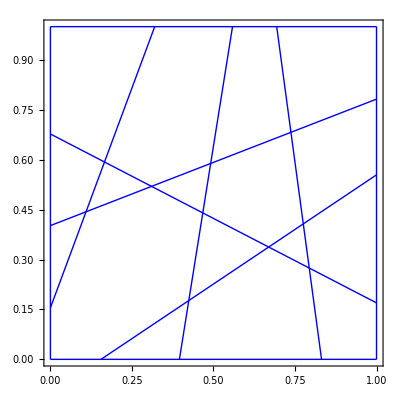

```mathematica
Module[{boundary,lines},
boundary=SquareVertices[1];
lines=MakeCourteousAnarchyLines[6,0.1,boundary,RandSeed->0];
Print["Found ",Length[lines]-Length[boundary]," lines"];
Graphics[Style[Line/@lines,Blue],Frame->True]
]
```

MakeCourteousAnarchyGraph[ngoal, mindist, boundary, opts] does the same thing but returns a TGraph of the Intersectified lines, suitable for feeding to MakeWovenTessellation.

```mathematica
MakeCourteousAnarchyGraph[ngoal_,mindist_,boundary_List,opts___]:=Module[{lines,verts,edges,tobj},
lines=MakeCourteousAnarchyLines[ngoal,mindist,boundary,opts];
{verts,edges}=Indexify[lines,2,opts];
tobj=MakeTGraph[verts,edges];
Intersectify[tobj]]
```

Example

```mathematica
Module[{boundary,tobj},
boundary=SquareVertices[1];
tobj=MakeCourteousAnarchyGraph[6,0.1,boundary,RandSeed->0];
GraphGraphics[tobj]
]//ShowExample
```

### Woven tessellation helpers

#### Notes

It’s often useful to compute an InsetSeparationPlot to determine the maximum inset distance possible for a given line pattern.

#### InsetSeparationFn[verts, edges] InsetSeparationPlot[tobj, {min, max}, opts] (checked class) TGraph

InsetSeparationFn[verts, edges] returns a pure function that gives the minimum inset point separation as a function of its argument. It is useful for finding the maximum inset distance for a given pattern.

```mathematica
InsetSeparationFn[verts_List,edges_List]:=Module[{tobj,faces,h,iverts,idists},
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph;
faces=GetValue[tobj,Faces];
iverts=Flatten[InsetPoly[verts⟦#⟧,h]&/@faces,1];
idists=Flatten[Table[Mag[iverts⟦i⟧-iverts⟦j⟧],{i,Length[iverts]},{j,i+1,Length[iverts]}],1];
Function[Evaluate[Min[idists]/.h->#]]]
```

Example

```mathematica
Module[{isfn},
isfn=InsetSeparationFn[{{0,0},{1,0},{1,1},{0,1}},{{1,2},{2,3},{3,4},{4,1}}];
Print[isfn];
isfn[0.4]
]//ShowExample
```

InsetSeparationPlot[tobj, {min, max}, opts] plots the inset separation over the range {min, max}. This lets us specify the exact inset distance to use in what is a computationally expensive calculation, MakeSimpleWovenTessellation.

```mathematica
InsetSeparationPlot[tobj_TObj,{min_,max_},opts___]:=Module[{isfn,verts,edges},
AssertClass[tobj,TGraph,InsetSeparationPlot];
{verts,edges}=GetValues[tobj,{Vertices,Edges}];
isfn=InsetSeparationFn[verts,edges];
Plot[isfn[x],{x,min,max}]
]
```

Example

```mathematica
Module[{verts,edges,tobj},
verts={{0,0},{1,0},{1,1},{0,1}};
edges={{1,2},{2,3},{3,4},{4,1}};
tobj=MakeTGraph[verts,edges];
GraphicsRow[{GenericGraphGraphics[verts,edges],
InsetSeparationPlot[tobj,{0,1.5}]}]
]//ShowExample
```

### Woven tessellation generation

#### Notes

The typical process for creating  woven tessellation is illustrated in the examples, but it basically follows this pattern:
(1) Generate a TGraph consisting of intersecting straight lines (e.g., via MakeChordStarGraph, MakeCourteousAnarchyGraph, or via your own algorithm).
(2) If necessary, Intersectify the TGraph to break it up into individual line segments.
(3) Create an InsetSepararationPlot of the graph to determine a suitable inset distance.
(4) Feed the graph to MakeSimpleWovenTessellation. The output is a TGraph2D that describes the crease pattern and folded form.

Mathematica 11 broke the original version of this function; I’ve rewritten part of the code to fix this.

In Tessellatica 11.1, I’ve updated this function to allow variable-width strips, not insetting the boundary, and, most significantly, added support for periodic boundary conditions. See the examples. Also fixed a minor bug that affected pleat width at the boundary.

#### MakeSimpleWovenTessellation[tobj, inset, opts] (checked class) TGraph (options) MinimumPleatSize, MinimumBorderPleatSize, WovenParity, WovenPeriodicity, StationaryFace, ShowProgress

MakeSimpleWovenTessellation[tobj, inset, opts] constructs a woven tessellation.

Arguments:
	tobj — a TGraph that specifies the original graph.
	inset — a constant inset distance or a list of insets, one for each line segment in the graph. Strip width is twice the inset distance.

Options:
	MinimumPleatSize → dmin, where dmin is the minimum pleat width relative to the inset distance. Default value is equal to the inset distance, i.e., 1.
	MinimumBorderPleatSize → dbmin, where dbmin is the minimum width of border pleats for diverging pleats, also relative to the inset distance. Default value is 0.01.
	BorderInset → Automatic | None, whether to inset the border by the same amount as the interior lines.
	WovenParity → ±1, which lets you switch the direction of the overlaps.
	WovenPeriodicity → None | {{i_1, j_1}, {i_2, j_2}, ...}, where the list of index pairs describes the desired periodicity of the pattern.
	StationaryFace → k, where k is the index of the face of the original graph to fix the position of; this determines the orientation of the crease pattern.
	ShowProgress→ True | False, if True, displays intermediate results. Very useful if you need to debug things.

Returns: a TGraph2D+TAssigned that describes the crease pattern and folded form.

The width of each woven strip is twice the inset distance inset. If inset is a list of values, then the width of each edge strip is given by its corresponding entry in inset. To avoid insetting the boundary edges, give a list of explicit inset distances and set all the edge inset values to zero.

BorderInset → Automatic will inset the border for non-periodic patterns (to be consistent with previous versions) but will not inset the border for periodic patterns.

If you use the WovenPeriodicity option, you will provide a structured list of indices that specifies the periodicity constraints, which you can use to create a version that tiles periodically. The specific form of this option is:
	WovenPeriodicity → {{i_1, j_1}, {i_2, j_2}...}
where each pair {i, j} are two vertices on the boundary that are periodic images of each other.

To construct the WovenPeriodicity conditions, run MakeSimpleWovenTessellation with ShowProgress turned on, then pick out the plot of “all new edges” to see vertex indices and how they are connected. Then you can re-run MakeSimpleWovenTessellation with the WovenPeriodicity data.

```mathematica
MinimumPleatSize::usage="MinimumPleatSize is an option to MakeSimpleWovenTessellation that specifies the minimum pleat width relative to the inset distance.";
```

```mathematica
MinimumBorderPleatSize::usage="MinimumBorderPleatSize is an option to MakeSimpleWovenTessellation that specifies the minimum width of border pleats for diverging pleats.";
```

```mathematica
WovenParity::usage="WovenParity is an option to MakeSimpleWovenTessellation that specifies the direction of the overlaps beteen the woven strips.";
```

```mathematica
WovenPeriodicity::usage="WovenPeriodicity is an option to MakeSimpleWovenTessellation that specifies whether and how the pattern should be periodic.";
```

```mathematica
BorderInset::usage="BorderInset is an option to MakeSimpleWovenTessellation tha specifies whether the border should be inset.";
```

```mathematica
Options[MakeSimpleWovenTessellation]={
MinimumPleatSize->1,
MinimumBorderPleatSize->0.01,
BorderInset->Automatic,
WovenParity->1,
WovenPeriodicity->None,
StationaryFace->1,
ShowProgress->False
};
```

```mathematica
MakeSimpleWovenTessellation::badbi="Option BorderInset → `1` must be either Automatic or None.";
```

```mathematica
MakeSimpleWovenTessellation::badper="Option WovenPeriodicity → `1` must be either None or a list of index pairs.";
```

```mathematica
MakeSimpleWovenTessellation::badins="Inset list `1` must have the same length as edge list `2`.";
```

```mathematica
MakeSimpleWovenTessellation::optfail="MakeSimpleWovenTessellation failed because it was unable to find a minimum in the optimization step.";
```

```mathematica
MakeSimpleWovenTessellation::nokawa="MakeSimpleWovenTessellation failed because the best solution found has a Kawasaki condition mismatch greater than 10^-4. Values were: `1`";
```

```mathematica
MakeSimpleWovenTessellation[tobj_TObj,inset_,opts___]:=Module[{mps,mbps,bi,wpar,wper,sface,sp,isper,tobjdef,verts,edges,faces,bverts,bedges,iedges,dedges,fei,vei,edgepairs,twocoloring,tcfv,h,insetverts,fvdata,beqv,beqe,di,db,makeverts,ndi,ndb,newverts,newfverts,newbverts,ocnmap,nwper,hdruleff,newedges,newtypes,nfvpos,prevnewvert,newvert,nextnewvert,altnewvert,prevvalvert,nextvalvert,addpleat,hdrulecp,tobjout,nedges,nbedges,niedges,vva,kawaconds,perconds,kawavals,merit,eqns,ineqns,vars,time,soln,newvertsff},
AssertClass[tobj,TGraph,MakeSimpleWovenTessellation];
mps=MinimumPleatSize/.{opts}/.Options[MakeSimpleWovenTessellation];
mbps=MinimumBorderPleatSize/.{opts}/.Options[MakeSimpleWovenTessellation];
bi=BorderInset/.{opts}/.Options[MakeSimpleWovenTessellation];
wpar=WovenParity/.{opts}/.Options[MakeSimpleWovenTessellation];
wper=WovenPeriodicity/.{opts}/.Options[MakeSimpleWovenTessellation];
sface=StationaryFace/.{opts}/.Options[MakeSimpleWovenTessellation];
sp=ShowProgress/.{opts}/.Options[MakeSimpleWovenTessellation];
If[!(bi===None||bi===Automatic),Message[MakeSimpleWovenTessellation::badbi,bi];Abort[]];
isper=!(wper===None);
If[isper&&!Head[wper]===List,Message[MakeSimpleWovenTessellation::badper,wper];Abort[]];

(* build the full primal-dual graph that we use to define the woven pattern *)
tobjdef=tobj//RebuildPlaneGraph//AddTPrimalDualGraph;
{verts,edges,faces,bverts,bedges,iedges,dedges,fei,vei}=GetValues[tobjdef,{Vertices,Edges,Faces,BoundaryVertices,BoundaryEdges,InteriorEdges,DualEdges,FaceEdgeIncidence,VertexEdgeIncidence}];
If[sp,Print["original pattern = ",GraphGraphics[tobjdef]]];
(* edgepairs *)
 edgepairs=OrientedInteriorEdgePairs[tobjdef];
If[sp,Print["edge pairs = ",edgepairs]];
(* two-coloring *)
twocoloring=TwoColorGraph[tobjdef,StartFace->wpar];
If[sp,Print["two-coloring = ",twocoloring,GenericGraphGraphics[verts,edges,faces,FaceColoring->twocoloring]]];
tcfv=MapThread[Table[#1,{Length[#2]}]&,{twocoloring,faces}];
If[sp,Print["two-coloring by vertex = ",tcfv]];

(* inset vertices *)
h=If[Head[inset]===List,
If[Length[inset]≠Length[edges],Message[MakeSimpleWovenTessellation::badins,inset,edges];Abort[]];inset,
Table[inset,{Length[edges]}]];
(* if we're specifying periodicity, set all boundary inset values to zero *)
If[isper||bi===None,(h⟦#⟧=0)&/@bedges];
insetverts=MapThread[InsetPoly[verts⟦#1⟧,h⟦#2⟧]&,{faces,fei}];
If[sp,Print["inset polygons = ",Graphics[{
{Black,Point/@verts},
{Red,Line[verts⟦#⟧&/@#]&/@edges},
{Green,Line[AppendFirst[#]]&/@insetverts}}]]];
(* Construct data describing the neighborhood of each vertex around each face: a list of data for each vertex, grouped by faces. *)
fvdata=Transpose/@Transpose[{
RotateRight/@faces(* prev vertex index *),
faces(* this vertex index *),
RotateLeft/@faces(* next vertex index *),
insetverts(* inset vertex coords *),
tcfv(* rotation direction *),
N/@NormalizeReal/@(verts⟦#⟧-verts⟦RotateRight[#]⟧)&/@faces(* prev edge vector *),
N/@NormalizeReal/@(verts⟦RotateLeft[#]⟧-verts⟦#⟧)&/@faces(* next edge vector *),
RotateRight/@fei(* prev edge index *),
fei(* next edge index *)}];
If[sp,Print["face/vertex data = ",fvdata]];

beqv[iseq___]:=And@@(MemberQ[bverts,#]&/@{iseq})(* tests if vertices are on boundary *);
beqe[ie_]:=MemberQ[bedges,ie](* tests if edge is on boundary *);
newverts={};
(* makeverts creates new vertices and returns list of new vertices associated with old ones. 
di[i] is the inset distance for an interior vertex.
db[i] is the inset distance for a border vertex. *)
makeverts[ip_,iv_,in_,ivert_,rot_,ep_,en_,iep_,ien_]:=Module[{csc,addi},
csc=1/Abs[en.Rotate90[ep]];
addi[]:=Length[AppendTo[newverts,ivert]];
Join[{iv},Which[
beqe[iep]&&beqe[ien],{addi[],0},
rot==1,Which[ 
beqe[iep],{Length[AppendTo[newverts,ivert+csc db[++ndb]ep h⟦ien⟧]],addi[]},
beqe[ien],{Length[AppendTo[newverts,ivert-csc db[++ndb] en h⟦iep⟧]],addi[]},
True,{Length[AppendTo[newverts,ivert-csc di[++ndi] en  h⟦iep⟧]],0}],
rot==-1,Which[
beqe[iep],{Length[AppendTo[newverts,ivert+csc db[++ndb]ep h⟦ien⟧]],addi[]},
beqe[ien],{Length[AppendTo[newverts,ivert-csc db[++ndb] en h⟦iep⟧]],addi[]},
True,{Length[AppendTo[newverts,ivert+csc di[++ndi]ep h⟦ien⟧]],0}],
True,Abort[] (* error! *)
]]];
ndi=0;
ndb=0;
(* We simultaneously build the new vertices (newverts) and a list of mappings from old vertices to new vertices, grouped by original faces (newfverts). Each triple {i,j,k} links old vertex i to new vertices j and k (k=0 if there's only one new vertex). *)
newfverts=Apply[makeverts,fvdata,{2}];
If[sp, Print["newfverts = ",newfverts]];
hdruleff={di[_]->0.7 ,db[_]->0.3 };
If[sp,Print["new vertices = ",Graphics[{
{Black,Point/@verts},
{Red,Line[verts⟦#⟧&/@#]&/@edges},
{Green,Line[AppendFirst[#]]&/@insetverts},
{Blue,Point/@newverts},
Style[StdVertexLabels[newverts],Blue]}]/.hdruleff]];

(* new boundary vertices *)
newbverts={};
If[beqv[#⟦1⟧],AppendTo[newbverts,#⟦2⟧];If[#⟦3⟧≠0,AppendTo[newbverts,#⟦3⟧]]]&/@Flatten[newfverts,1];
If[sp, Print["newbverts = ",newbverts]];

(* new periodicity pairs, if needed *)
If[isper,
(* A list of triples {oldvert, color, newvert}, used in periodicity *)
ocnmap=MapThread[{#1⟦1⟧,#2,#1⟦2⟧}&,{Flatten[newfverts,1],Flatten[tcfv,1]}];
If[sp,Print["old-color-new map = ",ocnmap]];
(* old periocity pairs and corresponding new vertex periodicity pairs *)
nwper=Flatten[Function[x,{{x,{Select[ocnmap,#⟦1⟧==x⟦1⟧&&#⟦2⟧==1&]⟦1,-1⟧,Select[ocnmap,#⟦1⟧==x⟦2⟧&&#⟦2⟧==1&]⟦1,-1⟧}},{x,{Select[ocnmap,#⟦1⟧==x⟦1⟧&&#⟦2⟧==-1&]⟦1,-1⟧,Select[ocnmap,#⟦1⟧==x⟦2⟧&&#⟦2⟧==-1&]⟦1,-1⟧}}}]/@wper,1];
If[sp,Print["new periodicity pairs = ",nwper]]];

(* new edges of the tessellation *)
newedges={};
newtypes={};
(AppendTo[newtypes,If[beqv[#⟦1,1⟧,#⟦2,1⟧],B,M]];AppendTo[newedges,{#⟦1,2⟧,#⟦2,2⟧}])&/@Transpose[{#,RotateLeft[#]}]&/@newfverts;
If[sp,Print["new edges = ",newedges]];
If[sp,Print["new types = ",newtypes]];
If[sp,Print["new edges (twist polygons) = ",Graphics[{
{Black,Point/@verts},
{Red,Line[verts⟦#⟧&/@#]&/@edges},
{Green,Line[AppendFirst[#]]&/@insetverts},
CreasePatternLines[MakeTGraph[newverts,newedges]//AddTAssignedTo[#,newtypes]&],
{Blue,Point/@newverts,StdVertexLabels[newverts]}
}]/.hdruleff/.OrigamiStyle[]]];
(* rest of the new edges *)
nfvpos[if_,iv_]:=Position[#⟦1⟧&/@newfverts⟦if⟧,iv]⟦1,1⟧;
prevnewvert[if_,iv_]:=RotateLeft[newfverts⟦if⟧,nfvpos[if,iv]-2]⟦1,2⟧;
newvert[if_,iv_]:=RotateLeft[newfverts⟦if⟧,nfvpos[if,iv]-1]⟦1,2⟧;
nextnewvert[if_,iv_]:=RotateLeft[newfverts⟦if⟧,nfvpos[if,iv]]⟦1,2⟧;
altnewvert[if_,iv_]:=RotateLeft[newfverts⟦if⟧,nfvpos[if,iv]-1]⟦1,3⟧;
prevvalvert[if_,iv_]:=If[#⟦3⟧≠0,#⟦3⟧,#⟦2⟧]&[RotateLeft[newfverts⟦if⟧,nfvpos[if,iv]-2]⟦1⟧];
nextvalvert[if_,iv_]:=If[#⟦3⟧≠0,#⟦3⟧,#⟦2⟧]&[RotateLeft[newfverts⟦if⟧,nfvpos[if,iv]]⟦1⟧];
addpleat[{{e1_,e2_},{fr_,fl_}}]:=(
(* creases near e1 *)
If[!MemberQ[bverts,e1],
(* e1 not on boundary *)
If[twocoloring⟦fl⟧==1,
AppendTo[newedges,{nextvalvert[fr,e1],prevvalvert[fl,e1]}];AppendTo[newtypes,V];AppendTo[newedges,{newvert[fr,e1],newvert[fl,e1]}];AppendTo[newtypes,M]],
(* e1 on the boundary *)
AppendTo[newedges,{newvert[fr,e1],altnewvert[fr,e1]}];AppendTo[newtypes,B];
AppendTo[newedges,{newvert[fl,e1],altnewvert[fl,e1]}];AppendTo[newtypes,B];
AppendTo[newedges,{altnewvert[fr,e1],altnewvert[fl,e1]}];AppendTo[newtypes,B];
If[twocoloring⟦fl⟧==-1,
AppendTo[newedges,{nextvalvert[fl,e1],altnewvert[fl,e1]}];AppendTo[newtypes,V];
AppendTo[newedges,{prevvalvert[fr,e1],altnewvert[fr,e1]}];AppendTo[newtypes,V]]];
(* creases near e2 *)
If[!MemberQ[bverts,e2],
(* e2 not on boundary *)
If[twocoloring⟦fl⟧==-1,
AppendTo[newedges,{prevvalvert[fr,e2],nextvalvert[fl,e2]}];AppendTo[newtypes,V];AppendTo[newedges,{newvert[fr,e2],newvert[fl,e2]}];AppendTo[newtypes,M]],
(* e2 on the boundary *)
AppendTo[newedges,{newvert[fr,e2],altnewvert[fr,e2]}];AppendTo[newtypes,B];
AppendTo[newedges,{newvert[fl,e2],altnewvert[fl,e2]}];AppendTo[newtypes,B];
AppendTo[newedges,{altnewvert[fr,e2],altnewvert[fl,e2]}];AppendTo[newtypes,B];
If[twocoloring⟦fl⟧==1,
AppendTo[newedges,{prevvalvert[fl,e2],altnewvert[fl,e2]}];AppendTo[newtypes,V];
AppendTo[newedges,{nextvalvert[fr,e2],altnewvert[fr,e2]}];AppendTo[newtypes,V]]];
);
addpleat/@Transpose[edgepairs];
If[sp,Print["all new edges = ",Graphics[{
{Black,Point/@verts},
{Red,Line[verts⟦#⟧&/@#]&/@edges},
{Green,Line[AppendFirst[#]]&/@insetverts},
CreasePatternLines[MakeTGraph[newverts,newedges]//AddTAssignedTo[#,newtypes]&],
{Blue,Point/@newverts,StdVertexLabels[newverts]}
}]/.hdruleff/.OrigamiStyle[]]];
(* That's everything; build TGraphs for crease pattern and folded form using unoptimized coordinates, then construct plane graph data so we have vertex adjacency for testing Kawasaki. *)
hdrulecp={di[_]->-0.1 ,db[_]->-0.1 };
tobjout=MakeTGraph[newverts/.hdrulecp, newedges];
If[sp,Print["topological CP (unoptimized) = ",GraphGraphics[tobjout]]];
tobjout=tobjout//AddTPlaneGraph//AddTAssigned[newtypes]//AddTGraph2D[newverts/.hdruleff];
If[sp,Print["topological FF (unoptimized) = ",Graph2DGraphics[tobjout]]];

(* if there's periodicity, get vertex indices at far end of edges in periodicity pairs *)
If[isper,
{nedges,nbedges}=GetValues[tobjout,{Edges,BoundaryEdges}];
niedges={}(* interior edges, as vertex pairs, both orders *);
Do[If[!ContainsQ[nbedges,i],AppendTo[niedges,nedges⟦i⟧]],{i,Length[nedges]}];
niedges=Join[niedges,Reverse/@niedges];
nwper=Function[x,Append[x,{Select[niedges,x⟦2,1⟧==#⟦1⟧&]⟦1,2⟧,Select[niedges,x⟦2,2⟧==#⟦1⟧&]⟦1,2⟧}]]/@nwper;
If[sp,Print["new periodicity data = ",nwper]];
];

(* PART 2: OPTIMIZATION *)

(* Kawasaki conditions. Note that FlatFoldabilityCondition gives the proper algebraic condition
on the FF vertices if they are given in their cyclic order of the CP. *)
kawaconds={};
vva=tobjout[VertexVertexAdjacency];
Do[If[Length[vva⟦i⟧]==4,AppendTo[kawaconds,FlatFoldabilityCondition[newverts⟦i⟧,newverts⟦vva⟦i⟧⟧]]],{i,Length[vva]}];
If[sp,Print["Kawasaki conditions (unoptimized) = ",kawaconds/.hdruleff]];

(* periodicity conditions, if applicable *)
If[isper,
perconds=Flatten[With[{dr=verts⟦#⟦1,2⟧⟧-verts⟦#⟦1,1⟧⟧},{(newverts⟦#⟦2,2⟧⟧-newverts⟦#⟦2,1⟧⟧-dr).(RotationMatrix2D[π/2].dr),TriangleSignedArea2D[newverts⟦#⟦3,1⟧⟧+dr,newverts⟦#⟦2,2⟧⟧,newverts⟦#⟦3,2⟧⟧]}]&/@nwper]];

(* optimization *)
vars=Join[Table[{di[i],mps},{i,ndi}],Table[{db[i],mbps},{i,ndb}]];
eqns=#==0&/@kawaconds;
If[isper,JoinTo[eqns,#==0&/@Drop[perconds,-1]]];
ineqns=Join[Table[di[i]≥mps,{i,ndi}],Table[db[i]≥mbps,{i,ndb}]];
merit=Sum[(di[i]^2),{i,ndi}]+Sum[(db[i]^2),{i,ndb}];
{time,soln}=Timing[FindMinimum[{merit,Join[eqns,ineqns]},vars]];
If[sp,Print["Optimization took ",time," seconds."]];
If[Head[soln]===FindMinimum,Message[MakeSimpleWovenTessellation::optfail];Abort[]];
If[sp,PrintThis[soln]];
kawavals=kawaconds/.soln⟦2⟧;
If[sp,Print["Kawasaki conditions (optimized) = ",Chop[kawavals]]];
(* If mismatch, don't abort, but report the mismatch *)
If[Max[Abs/@kawavals]>10^-4,Message[MakeSimpleWovenTessellation::nokawa,kawavals]];
If[sp,Print["periodic conditions (optimized) = ",Chop[perconds/.soln⟦2⟧]]];
newvertsff=newverts/.soln⟦2⟧;

(* build proper embedding based on the solution *)
tobjout=tobjout//ReplaceProperty[Vertices2D->newvertsff];
tobjout=UnfoldGraph2D[tobjout,StationaryFace->sface];
If[sp,Print["topological crease pattern and folded form (optimized)"];
Print[GraphicsRow[{GraphGraphics[tobjout],Graph2DGraphics[tobjout]}]];
Print[GraphicsRow[{CreasePatternGraphics[tobjout],GenericFoldedFormGraphics[tobjout]}]/.OrigamiStyle[]]];
tobjout]
```

### Woven tessellation examples

#### Three lines

This example shows how to build a woven tessellation from a graph of intersecting line segments.

In this example, we’ll show the CP from the back side but the FF from the front. We make use of a trick to render the folded form: the last face built is one of the “sliver” faces, so we’ll use that index as the value of FaceupFace for a properly rendered flopped image.

```mathematica
Module[{verts,edges,tobj,tobjw},
verts={{0,0},{1,0},{3,0},{4,0},{0,1},{1,1},{2,1},{4,1},{1,2},{0,3},{0,4},{1,4},{4,4}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8},{5,10},{6,9},{7,9},{8,13},{9,10},{10,11},{9,12},{11,12},{12,13}};
tobj=MakeTGraph[verts,edges];
Print[GraphGraphics[tobj]];
tobjw=MakeSimpleWovenTessellation[tobj,0.20,WovenParity->1,StationaryFace->6,BorderInset->None,ShowProgress->False];
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Four lines

This example shows how to build a woven tessellation from a manually built set of intersecting lines and boundary. We build a set of lines, Intersectify them, to make the TGraph, then feed it to MakeWovenTessellation. Again, we flop the folded form.

```mathematica
Module[{sgverts,sgedges,tobjcsg,tobj,tobjw},
(* Make a graph *)
sgverts={
{0,0},{1,0},{1.5,0},{2,0},
{0,0.5},{2,0.5},
{0,0.9},{2,0.9},
{0,1.5},{1,1.5},{1.5,1.5},{2,1.5}};
sgedges={{1,4},{5,6},{7,8},{9,12},{1,9},{2,10},{3,11},{4,12}};
tobjcsg=MakeTGraph[sgverts,sgedges];
(* Intersectify to break it into individual line segments *)
tobj=Intersectify[tobjcsg];
Print[GraphicsRow[{GraphGraphics[tobjcsg],GraphGraphics[tobj]}]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobj,{0.,0.3}]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellation[tobj,0.1,WovenParity->-1,BorderInset->None];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Four lines, variable widths

This example shows off the new variable line width function. Note that the list of inset distances, hlist, must correspond with the edges of the intersectified line set and should be consistent along any collinear group of line segments.

```mathematica
Module[{sgverts,sgedges,tobjcsg,tobj,hlist,tobjw},
(* Make a graph *)
sgverts={
{0,0},{1,0},{1.5,0},{2,0},
{0,0.5},{2,0.5},
{0,0.9},{2,0.9},
{0,1.5},{1,1.5},{1.5,1.5},{2,1.5}};
sgedges={{1,4},{5,6},{7,8},{9,12},{1,9},{2,10},{3,11},{4,12}};
tobjcsg=MakeTGraph[sgverts,sgedges];
(* Intersectify to break it into individual line segments *)
tobj=Intersectify[tobjcsg];
Print[GraphicsRow[{GraphGraphics[tobjcsg],GraphGraphics[tobj]}]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobj,{0.,0.3}]]//Hold;
(* create a list of varying inset distances *)
hlist={0,0,0,.2,.2,.2,.1,.1,.1,0,0,0,0,0,0,.2,.2,.2,.1,.1,.1,0,0,0};
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellation[tobj,hlist,WovenParity->-1,BorderInset->None];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Four lines, periodic

This example shows four lines but now includes WovenPeriodicity data the specifies that the pattern is periodic.

```mathematica
Module[{sgverts,sgedges,tobjcsg,tobj,wper,tobjw},
(* Make a graph *)
sgverts={
{0,0},{1,0},{1.5,0},{2,0},
{0,0.5},{2,0.5},
{0,0.9},{2,0.9},
{0,1.5},{1,1.5},{1.5,1.5},{2,1.5}};
sgedges={{1,4},{5,6},{7,8},{9,12},{1,9},{2,10},{3,11},{4,12}};
tobjcsg=MakeTGraph[sgverts,sgedges];
(* Intersectify to break it into individual line segments *)
tobj=Intersectify[tobjcsg];
Print[GraphicsRow[{GraphGraphics[tobjcsg],GraphGraphics[tobj]}]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobj,{0.,0.3}]]//Hold;
(* set up woven perodicity data *)
wper={{2,14},{3,15},{5,8},{9,12}};
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellation[tobj,.15,WovenParity->-1,WovenPeriodicity->wper,ShowProgress->False];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Four lines, periodic, non-crossing line

This example includes a line segment that doesn’t cross any others, a situation that arises for some periodic patterns.

We’ll use GenericFoldedFormGraphics for the folded form because the non-crossing line confuses VisibleFoldedFormGraphics when it tries to render hidden lines.

```mathematica
Module[{verts,edges,tobj,wper,tobjw,tobjwf},
verts={{0,0},{1,0},{3,0},{4,0},{0,1},{1,1},{2,1},{4,1},{1,2},{0,3},{4,3},{0,4},{1,4},{3,4},{4,4}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8},{5,10},{6,9},{7,9},{8,11},{9,10},{9,13},{10,12},{11,14},{11,15},{12,13},{13,14},{14,15}};
tobj=MakeTGraph[verts,edges];
Print[GraphGraphics[tobj]];
wper={{5,8},{2,13},{3,14},{10,11}};
tobjw=MakeSimpleWovenTessellation[tobj,0.20,WovenParity->1,WovenPeriodicity->wper,MinimumBorderPleatSize->.01,StationaryFace->6,ShowProgress->False];
tobjwf=FlopGraph2D[tobjw];
GraphicsRow[{
CreasePatternGraphics[tobjwf],
GenericFoldedFormGraphics[tobjwf]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Regular 7-star

This example shows the progressive construction of a regular 7-star from a chord star graph.

Display with generic folded form because of irreconcilable overlaps.

```mathematica
Module[{tobjcsg,tobjw},
(* Make a chord star graph *)
tobjcsg=MakeChordStarGraph[{{0°,0.15}},7];
Print[GraphGraphics[tobjcsg]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobjcsg,{0.,0.04}]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellation[tobjcsg,0.03,WovenParity->-1];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
GenericFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### 2-layer 6-fold star

Another from a chord star graph with 6-fold rotation and 2 layers of lines. Takes a while to compute and render, so we’ll turn on ShowProgress.

Also use GenericFoldedFormGraphics because of overlaps.

```mathematica
Module[{tobjcsg,tobjw},
(* Make a chord star graph *)
tobjcsg=MakeChordStarGraph[{{30°,0.4},{0°,0.3}},6];
Print[GraphGraphics[tobjcsg]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobjcsg,{0.,0.04}]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellation[tobjcsg,0.024,WovenParity->1,ShowProgress->True];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
GenericFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Courteous anarchy

A small example of courteous anarchy.

```mathematica
Module[{boundary,lines,verts,edges,tobj,tobjw},
boundary=SquareVertices[1];
tobj=MakeCourteousAnarchyGraph[6,0.1,boundary,RandSeed->0];
Print[GraphGraphics[tobj]];
Print[InsetSeparationPlot[tobj,{0.,0.07}]];
tobjw=MakeSimpleWovenTessellation[tobj,0.035,WovenParity->-1];
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Dislocation

Show progress on this one.

```mathematica
Module[{tobj,tobjcsg,tobjw},
tobj=MakeTGraph@@{{{1.2423,1.1112},{1.2423,353.20419999999996},{77.6633,1.1112},{77.6633,353.20419999999996},{144.0843,1.1112},{144.0843,353.20419999999996},{210.50530000000003,1.1112},{210.50530000000003,353.20419999999996},{276.92530000000005,1.1112},{276.92530000000005,353.20419999999996},{353.34630000000004,1.1112},{353.34630000000004,353.20419999999996},{1.2424000000000335,77.5322},{353.34540000000004,77.5222},{1.2415000000000336,143.9532},{353.34450000000004,143.94320000000002},{1.2403000000000335,210.37420000000003},{353.34330000000006,210.36420000000004},{1.2394000000000336,276.7952},{353.34240000000005,276.78520000000003},{39.001500000000036,353.21520000000004},{353.34650000000005,32.00220000000007}},{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{1,11},{13,14},{15,16},{17,18},{19,20},{2,12},{21,22}}};
Print[GraphGraphics[tobj]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobj,{0.,10.,0.5}]];
(* make our woven tessellation *)
tobjcsg=Intersectify[tobj,IntersectionTolerance->2,SamePtTolerance->2]//AddTPlaneGraph;
Print[GraphGraphics[tobjcsg]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellation[tobjcsg,8.,WovenParity->1,ShowProgress->True];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
(CreasePatternGraphics[tobjw]//InvertFoldType)/.OrigamiStyle[]
]//ShowExample
```

### Original version

#### MakeSimpleWovenTessellationOld[tobj, inset, opts] (checked class) TGraph (options) MinimumPleatSize, MinimumBorderPleatSize, WovenParity, StationaryFace, ShowProgress

MakeSimpleWovenTessellationOld[tobj, inset, opts] constructs a woven tessellation from a TGraph tobj and inset distance inset, and returns a TGraph2D+TAssigned that describe the crease pattern and folded form. The width of the woven strips is twice the inset distance inset.

Options:
	MinimumPleatSize → dmin, where dmin is the minimum pleat width relative to the inset distance. Default value is equal to the inset distance, i.e., 1.
	MinimumBorderPleatSize →dbmin, where dbmin is the minimum width of border pleats for diverging pleats, also relative to the inset distance. Default value is 0.01.
	WovenParity →±1, which lets you switch the direction of the overlaps.
	StationaryFace →k, where k is the index of the face of the original graph to hold stationary; this gives a preferred orientation to the crease pattern.
	ShowProgress→True | False, if True, displays intermediate results. Very useful if you need to debug things.

```mathematica
Options[MakeSimpleWovenTessellationOld]={
MinimumPleatSize->1,
MinimumBorderPleatSize->0.01,
WovenParity->1,
StationaryFace->1,
ShowProgress->False
};
```

```mathematica
MakeSimpleWovenTessellationOld::optfail="MakeSimpleWovenTessellationOld failed because it was unable to find a minimum in the optimization step.";
```

```mathematica
MakeSimpleWovenTessellationOld::nokawa="MakeSimpleWovenTessellationOld failed because the best solution found has a Kawasaki condition mismatch greater than 10^-4. Values were: `1`";
```

```mathematica
MakeSimpleWovenTessellationOld[tobj_TObj,inset_,opts___]:=Module[{mps,mbps,wpar,sface,sp,tobjdef,verts,edges,faces,boundary,iedges,dedges,edgepairs,twocoloring,h,insetverts,facedata,beq,d,dd,makenewvert,nd,ndd,newverts,newfaceverts,newboundaryverts,hdruleff,newedges,newtypes,prevnewvert,newvert,nextnewvert,altnewvert,prevvalvert,nextvalvert,addpleat,hdrulecp,tobjout,vva,kawaconds,kawavals,merit,eqns,ineqns,vars,time,soln,newvertsff},
AssertClass[tobj,TGraph,MakeSimpleWovenTessellationOld];
mps=MinimumPleatSize/.{opts}/.Options[MakeSimpleWovenTessellationOld];
mbps=MinimumBorderPleatSize/.{opts}/.Options[MakeSimpleWovenTessellationOld];
wpar=WovenParity/.{opts}/.Options[MakeSimpleWovenTessellationOld];
sface=StationaryFace/.{opts}/.Options[MakeSimpleWovenTessellationOld];
sp=ShowProgress/.{opts}/.Options[MakeSimpleWovenTessellationOld];
(* build the full primal-dual graph that we use to define the woven pattern *)
tobjdef=AddTPlaneGraphTo[tobj]//AddTPrimalDualGraphTo;
{verts,edges,faces,boundary,iedges,dedges}=GetValues[tobjdef,{Vertices,Edges,Faces,BoundaryVertices,InteriorEdges,DualEdges}];
If[sp,Print["original pattern = ",GraphGraphics[tobjdef]]];
(* edgepairs *)
 edgepairs=OrientedInteriorEdgePairs[tobjdef];
If[sp,PrintThis[edgepairs]];
(* build the two-coloring *)
twocoloring=TwoColorGraph[tobjdef,StartFace->(wpar)(sface)];
If[sp,PrintThis[twocoloring]];
(* inset vertices *)
insetverts=InsetPoly[verts⟦#⟧,h]&/@faces;
If[sp,Print["inset polygons = ",Graphics[{{Black,Point/@verts},{Red,Line[verts⟦#⟧&/@#]&/@edges},{Green,Line[AppendFirst[#]]&/@insetverts}}]/.h->inset]];
(* new vertices of the tessellation *)
facedata=Transpose/@Transpose[{
RotateRight/@faces,
faces,
RotateLeft/@faces,
insetverts,
MapThread[Table[#1,{Length[#2]}]&,{twocoloring,faces}],
N/@NormalizeReal/@(verts⟦#⟧-verts⟦RotateRight[#]⟧)&/@faces,
N/@NormalizeReal/@(verts⟦RotateLeft[#]⟧-verts⟦#⟧)&/@faces
}];
beq=MemberQ[boundary,#1]&&MemberQ[boundary,#2]&;
makenewvert[ip_,iv_,in_,ivert_,rot_,ep_,en_]:=Module[{csc},
csc=1/Abs[en.Rotate90[ep]];
Join[{iv},Which[
beq[ip,iv]&&beq[iv,in],{Length[AppendTo[newverts,ivert]],0},
rot==1,Which[ 
beq[ip,iv],{Length[AppendTo[newverts,ivert+csc dd[++ndd]ep]],Length[AppendTo[newverts,ivert]]},
beq[iv,in],{Length[AppendTo[newverts,ivert-csc d[++nd] en]],Length[AppendTo[newverts,ivert]]},
True,{Length[AppendTo[newverts,ivert-csc d[++nd] en]],0}],
rot==-1,Which[
beq[ip,iv],{Length[AppendTo[newverts,ivert+csc d[++nd]ep]],Length[AppendTo[newverts,ivert]]},
beq[iv,in],{Length[AppendTo[newverts,ivert-csc dd[++ndd] en]],Length[AppendTo[newverts,ivert]]},
True,{Length[AppendTo[newverts,ivert+csc d[++nd]ep]],0}],
True,Abort[] (* error! *)
]]];
nd=0;
ndd=0;
newverts={};
newfaceverts=Apply[makenewvert,facedata,{2}];
newboundaryverts={};
If[MemberQ[boundary,#⟦1⟧],AppendTo[newboundaryverts,#⟦2⟧];If[#⟦3⟧≠0,AppendTo[newboundaryverts,#⟦3⟧]]]&/@Flatten[newfaceverts,1];
hdruleff={h->inset,d[_]->0.8 inset,dd[_]->0.2 inset};
If[sp,Print["new vertices = ",Graphics[{{Black,Point/@verts},{Red,Line[verts⟦#⟧&/@#]&/@edges},{Green,Line[AppendFirst[#]]&/@insetverts},{Blue,Point/@newverts}}]/.hdruleff]];
(* new edges of the tessellation *)
newedges={};
newtypes={};
(AppendTo[newtypes,If[beq[#⟦1,1⟧,#⟦2,1⟧],B,M]];AppendTo[newedges,{#⟦1,2⟧,#⟦2,2⟧}])&/@Transpose[{#,RotateLeft[#]}]&/@newfaceverts;
If[sp,PrintThis[newedges]];
If[sp,PrintThis[newtypes]];
If[sp,Print["new edges (twist polygons) = ",Graphics[{
{Black,Point/@verts},
{Red,Line[verts⟦#⟧&/@#]&/@edges},
{Green,Line[AppendFirst[#]]&/@insetverts},
CreasePatternLines[MakeTGraph[newverts,newedges]//AddTAssignedTo[#,newtypes]&],
{Blue,Point/@newverts,StdVertexLabels[newverts]}
}]/.hdruleff/.OrigamiStyle[]]];
(* rest of the new edges *)
prevnewvert[if_,iv_]:=RotateLeft[newfaceverts⟦if⟧,Position[#⟦1⟧&/@newfaceverts⟦if⟧,iv]⟦1,1⟧-2]⟦1,2⟧;
newvert[if_,iv_]:=RotateLeft[newfaceverts⟦if⟧,Position[#⟦1⟧&/@newfaceverts⟦if⟧,iv]⟦1,1⟧-1]⟦1,2⟧;
nextnewvert[if_,iv_]:=RotateLeft[newfaceverts⟦if⟧,Position[#⟦1⟧&/@newfaceverts⟦if⟧,iv]⟦1,1⟧]⟦1,2⟧;
altnewvert[if_,iv_]:=RotateLeft[newfaceverts⟦if⟧,Position[#⟦1⟧&/@newfaceverts⟦if⟧,iv]⟦1,1⟧-1]⟦1,3⟧;
prevvalvert[if_,iv_]:=If[#⟦3⟧≠0,#⟦3⟧,#⟦2⟧]&[RotateLeft[newfaceverts⟦if⟧,Position[#⟦1⟧&/@newfaceverts⟦if⟧,iv]⟦1,1⟧-2]⟦1⟧];
nextvalvert[if_,iv_]:=If[#⟦3⟧≠0,#⟦3⟧,#⟦2⟧]&[RotateLeft[newfaceverts⟦if⟧,Position[#⟦1⟧&/@newfaceverts⟦if⟧,iv]⟦1,1⟧]⟦1⟧];
addpleat[{{e1_,e2_},{fr_,fl_}}]:=(
(* creases near e1 *)
If[!MemberQ[boundary,e1],
(* e1 not on boundary *)
If[twocoloring⟦fl⟧==1,
AppendTo[newedges,{nextvalvert[fr,e1],prevvalvert[fl,e1]}];AppendTo[newtypes,V];AppendTo[newedges,{newvert[fr,e1],newvert[fl,e1]}];AppendTo[newtypes,M]],
(* e1 on the boundary *)
AppendTo[newedges,{newvert[fr,e1],altnewvert[fr,e1]}];AppendTo[newtypes,B];
AppendTo[newedges,{newvert[fl,e1],altnewvert[fl,e1]}];AppendTo[newtypes,B];
AppendTo[newedges,{altnewvert[fr,e1],altnewvert[fl,e1]}];AppendTo[newtypes,B];
If[twocoloring⟦fl⟧==-1,
AppendTo[newedges,{nextvalvert[fl,e1],altnewvert[fl,e1]}];AppendTo[newtypes,V];
AppendTo[newedges,{prevvalvert[fr,e1],altnewvert[fr,e1]}];AppendTo[newtypes,V]]];
(* creases near e2 *)
If[!MemberQ[boundary,e2],
(* e2 not on boundary *)
If[twocoloring⟦fl⟧==-1,
AppendTo[newedges,{prevvalvert[fr,e2],nextvalvert[fl,e2]}];AppendTo[newtypes,V];AppendTo[newedges,{newvert[fr,e2],newvert[fl,e2]}];AppendTo[newtypes,M]],
(* e2 on the boundary *)
AppendTo[newedges,{newvert[fr,e2],altnewvert[fr,e2]}];AppendTo[newtypes,B];
AppendTo[newedges,{newvert[fl,e2],altnewvert[fl,e2]}];AppendTo[newtypes,B];
AppendTo[newedges,{altnewvert[fr,e2],altnewvert[fl,e2]}];AppendTo[newtypes,B];
If[twocoloring⟦fl⟧==1,
AppendTo[newedges,{prevvalvert[fl,e2],altnewvert[fl,e2]}];AppendTo[newtypes,V];
AppendTo[newedges,{nextvalvert[fr,e2],altnewvert[fr,e2]}];AppendTo[newtypes,V]]];
);
addpleat/@Transpose[edgepairs];
If[sp,Print["all new edges = ",Graphics[{
{Black,Point/@verts,StdVertexLabels[verts]},
{Red,Line[verts⟦#⟧&/@#]&/@edges,StdEdgeLabels[verts,edges]},
{Green,Line[AppendFirst[#]]&/@insetverts,Darker[Green],StdFaceLabels[verts,faces]},
CreasePatternLines[MakeTGraph[newverts,newedges]//AddTAssignedTo[#,newtypes]&],
{Blue,Point/@newverts,StdVertexLabels[newverts]}
}]/.hdruleff/.OrigamiStyle[]]];

(* That's everything; build TGraphs for crease pattern and folded form using unoptimized coordinates *)
hdrulecp={h->0.45 inset,d[_]->-0.45 inset,dd[_]->-0.05 inset};
tobjout=MakeTGraph[newverts/.hdrulecp, newedges]//AddTPlaneGraphTo//AddTAssignedTo[#,newtypes]&//AddTGraph2D[newverts/.hdruleff];
If[sp,Print["topological crease pattern and folded form (unoptimized)"];
Print[GraphicsRow[{GraphGraphics[tobjout],Graph2DGraphics[tobjout]}]]];

(* PART 2: OPTIMIZATION *)

(* Kawasaki conditions *)
(* Note that FlatFoldabilityCondition gives the proper algebraic condition
on the FF vertices if they are given in their cyclic order of the CP. *)
vva=tobjout[VertexVertexAdjacency];
kawaconds={};
Do[If[Length[vva⟦i⟧]==4,AppendTo[kawaconds,FlatFoldabilityCondition[newverts⟦i⟧,newverts⟦vva⟦i⟧⟧]]],{i,Length[vva]}];
If[sp,Print["Kawasaki conditions (unoptimized) = ",kawaconds/.hdruleff]];

(* optimization *)
merit=Sum[(d[i]^2),{i,nd}]+Sum[(dd[i]^2),{i,ndd}];
eqns=#==0&/@kawaconds/.h->inset;
ineqns=Join[Table[d[i]≥mps h,{i,nd}],Table[dd[i]≥mbps h,{i,ndd}]]/.h->inset;
vars=Join[Table[{d[i],mps h},{i,nd}],Table[{dd[i],mbps h},{i,ndd}]]/.h->inset;
{time,soln}=Timing[FindMinimum[{merit,Join[eqns,ineqns]},vars]];
If[sp,Print["Optimization took ",time," seconds."]];
If[Head[soln]===FindMinimum,Message[MakeSimpleWovenTessellationOld::optfail];Abort[]];
If[sp,PrintThis[soln]];
kawavals=kawaconds/.h->inset/.soln⟦2⟧;
If[sp,Print["Kawasaki conditions (optimized) = ",Chop[kawavals]]];
(* If mismatch, don't abort, but report the mismatch *)
If[Max[Abs/@kawavals]>10^-4,Message[MakeSimpleWovenTessellationOld::nokawa,kawavals]];
newvertsff=newverts/.h->inset/.soln⟦2⟧;

(* build proper embedding based on the solution *)
tobjout=tobjout//ReplaceProperty[Vertices2D->newvertsff];
tobjout=UnfoldGraph2D[tobjout,StationaryFace->sface];
If[sp,Print["topological crease pattern and folded form (optimized)"];
Print[GraphicsRow[{GraphGraphics[tobjout],Graph2DGraphics[tobjout]}]]];
If[sp,Print[GraphicsRow[{
CreasePatternGraphics[tobjout],
GenericFoldedFormGraphics[tobjout]
}]/.OrigamiStyle[]]];
tobjout]
```

#### Three lines

This example shows how to build a woven tessellation from a graph of intersecting line segments.

Note that you can turn on ShowProgress to display progress images and data. In this example, we’ll show the CP from the back side but the FF from the front. We make use of a trick to render the folded form: the last face built is one of the “sliver” faces, so we’ll use that index as the value of FaceupFace for a properly rendered flopped image.

```mathematica
Module[{verts,edges,tobj,tobjw},
verts={{0,0},{1,0},{3,0},{4,0},{0,1},{1,1},{2,1},{4,1},{1,2},{0,3},{0,4},{1,4},{4,4}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8},{5,10},{6,9},{7,9},{8,13},{9,10},{10,11},{9,12},{11,12},{12,13}};
tobj=MakeTGraph[verts,edges];
Print[GraphGraphics[tobj]];
tobjw=MakeSimpleWovenTessellationOld[tobj,0.20,WovenParity->1,StationaryFace->6,ShowProgress->False];
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Four orthogonal lines

This example shows how to build a woven tessellation from a manually built set of intersecting lines and boundary. We build a set of lines, Intersectify them, to make the TGraph, then feed it to MakeWovenTessellation. Again, we flop the folded form.

```mathematica
Module[{sgverts,sgedges,tobjcsg,tobj,tobjw},
(* Make a graph *)
sgverts={
{0,0},{1,0},{1.5,0},{2,0},
{0,0.5},{2,0.5},
{0,0.9},{2,0.9},
{0,1.5},{1,1.5},{1.5,1.5},{2,1.5}};
sgedges={{1,4},{5,6},{7,8},{9,12},{1,9},{2,10},{3,11},{4,12}};
tobjcsg=MakeTGraph[sgverts,sgedges];
(* Intersectify to break it into individual line segments *)
tobj=Intersectify[tobjcsg];
Print[GraphicsRow[{GraphGraphics[tobjcsg],GraphGraphics[tobj]}]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobj,{0.,0.3}]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellationOld[tobj,0.1,WovenParity->-1];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Regular 7-star

This example shows the progressive construction of a regular 7-star from a chord star graph.

Display with generic folded form because of irreconcilable overlaps.

```mathematica
Module[{tobjcsg,tobjw},
(* Make a chord star graph *)
tobjcsg=MakeChordStarGraph[{{0°,0.15}},7];
Print[GraphGraphics[tobjcsg]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobjcsg,{0.,0.04}]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellationOld[tobjcsg,0.03,WovenParity->-1];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
GenericFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### 2-layer 6-fold star

Another from a chord star graph with 6-fold rotation and 2 layers of lines. Takes a while to compute and render, so we’ll turn on ShowProgress.

Also use GenericFoldedFormGraphics because of overlaps.

```mathematica
Module[{tobjcsg,tobjw},
(* Make a chord star graph *)
tobjcsg=MakeChordStarGraph[{{30°,0.4},{0°,0.3}},6];
Print[GraphGraphics[tobjcsg]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobjcsg,{0.,0.04}]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellationOld[tobjcsg,0.024,WovenParity->1,ShowProgress->True];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
GraphicsRow[{
CreasePatternGraphics[tobjw],
GenericFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample
```

#### Courteous anarchy

A small example of courteous anarchy.

TBD: the root-finder now fails on this one. (Used to work in Mathematica 10.)

```mathematica
Module[{boundary,lines,verts,edges,tobj,tobjw},
boundary=SquareVertices[1];
tobj=MakeCourteousAnarchyGraph[6,0.1,boundary,RandSeed->0];
Print[GraphGraphics[tobj]];
Print[InsetSeparationPlot[tobj,{0.,0.07}]];
tobjw=MakeSimpleWovenTessellationOld[tobj,0.035,WovenParity->-1];
GraphicsRow[{
CreasePatternGraphics[tobjw],
VisibleFoldedFormGraphics[FlopGraph2D[tobjw],FaceupFace->Length[GetValue[tobjw,Faces]]]
}]/.OrigamiStyle[]
]//ShowExample//Hold;(* Root-finder now fails. Used to work in Ma10, but fails il Ma11, Ma12 *)
```

#### Dislocation

```mathematica
Module[{tobj,tobjcsg,tobjw},
tobj=MakeTGraph@@{{{1.2423,1.1112},{1.2423,353.20419999999996},{77.6633,1.1112},{77.6633,353.20419999999996},{144.0843,1.1112},{144.0843,353.20419999999996},{210.50530000000003,1.1112},{210.50530000000003,353.20419999999996},{276.92530000000005,1.1112},{276.92530000000005,353.20419999999996},{353.34630000000004,1.1112},{353.34630000000004,353.20419999999996},{1.2424000000000335,77.5322},{353.34540000000004,77.5222},{1.2415000000000336,143.9532},{353.34450000000004,143.94320000000002},{1.2403000000000335,210.37420000000003},{353.34330000000006,210.36420000000004},{1.2394000000000336,276.7952},{353.34240000000005,276.78520000000003},{39.001500000000036,353.21520000000004},{353.34650000000005,32.00220000000007}},{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{1,11},{13,14},{15,16},{17,18},{19,20},{2,12},{21,22}}};
Print[GraphGraphics[tobj]];
(* plot the inset separation to find an aesthetically pleasing strip width *)
Print[InsetSeparationPlot[tobj,{0.,10.,0.5}]];
(* make our woven tessellation *)
tobjcsg=Intersectify[tobj,IntersectionTolerance->2,SamePtTolerance->2]//AddTPlaneGraph;
Print[GraphGraphics[tobjcsg]];
(* build the new woven tessellation *)
tobjw=MakeSimpleWovenTessellationOld[tobjcsg,8.,WovenParity->1,ShowProgress->True];
(* Turn over the folded form, i.e., invert the crease assignment and flop the image. *)
temp=(CreasePatternGraphics[tobjw]//InvertFoldType)/.OrigamiStyle[]
]//ShowExample
```

## Rotationally symmetric pots

### Rotationally symmetric polyhedra

#### Notes

These functions are useful for generating explanatory figures. They’re not actually used for crease patterns.

#### SingleGoreData[pts, m]

SingleGoreData[pts, m] takes a list pts of {x, z} pairs defining a cross section and returns a list {t3d, r3d, c3d, u2d} of Graphics3D or Graphics elements that describe a single gore of an m-fold rotational solid, where:
	t3d is the gore curved in 3D as a Graphics3D Polygon
	r3d is the gore flattened in the x-y plane, as a Graphics3D Polygon
	c3d is the gore flattened vertically at the radial distance of the maximum x-value in pts, as a Graphics3D Polygon
	u2d is the gore flattened into 2D, as a Graphics2D Polygon

```mathematica
SingleGoreData[pts_List,m_]:=Module[{ϕ,x,z,r,w,nr,a,b,c,t3d,r3d,c3d,u2d},
ϕ=π/m;
{x,z}=Transpose[pts];
r=Prepend[Accumulate[Mag/@(Drop[pts,1]-Drop[pts,-1])],0];
nr=Length[r];
w=Tan[ϕ]x;
(* folded form points in 3D *)
a={#⟦1⟧,0,#⟦2⟧}&/@pts;
b=a+(U3D[π/2]#&/@w);
t3d=Table[Polygon[{b⟦i⟧,b⟦i+1⟧,{1,-1,1}b⟦i+1⟧,{1,-1,1}b⟦i⟧}],{i,nr-1}];
(* crease pattern points in 3D, radial *)
a={#,0,0}&/@r;
b=a+(U3D[π/2]#&/@w);
r3d=Table[Polygon[{b⟦i⟧,b⟦i+1⟧,{1,-1,1}b⟦i+1⟧,{1,-1,1}b⟦i⟧}],{i,nr-1}];
(* crease pattern points in 3D, cylindrical *)
a={Max[First/@pts],0,#+1-r⟦-1⟧/2}&/@r;
b=a+(U3D[π/2]#&/@w);
c3d=Table[Polygon[{b⟦i⟧,b⟦i+1⟧,{1,-1,1}b⟦i+1⟧,{1,-1,1}b⟦i⟧}],{i,nr-1}];
(* flat gore in 2D *)
c=#⟦{3,2}⟧&/@b;
c=#-c⟦1⟧&/@c;
u2d=Table[Line[Join[c,Reverse[{1,-1}#&/@c]]],{i,nr}];
{t3d,r3d,c3d,u2d}]
```

Example

```mathematica
Module[{n,pts,m,t3d,r3d,c3d,u2d},
n=8;
pts=Table[{Sin[ϕ],1-Cos[ϕ]},{ϕ,0,π,π/n}]//N;
m=8;
{t3d,r3d,c3d,u2d}=SingleGoreData[pts,m];
GraphicsGrid[{{
Graphics3D[t3d,Axes->True],
Graphics3D[r3d,Axes->True]},{
Graphics3D[c3d,Axes->True],
Graphics[u2d,Axes->True]}}]
]//ShowExample
```

#### MultipleGoreData[pts, m]

MultipleGoreData[pts, m] returns the same type of list as SingleGoreData, but now each element of the return list consists of all m gores.

```mathematica
MultipleGoreData[pts_List,m_]:=Module[{t3d,r3d,c3d,u2d},
{t3d,r3d,c3d,u2d}=SingleGoreData[pts,m];
{Table[RotateZ3D[ t3d,2  j π/m],{j,0,m-1}],
Table[RotateZ3D[ r3d,2  j π/m],{j,0,m-1}],
Table[RotateZ3D[ c3d,2  j π/m],{j,0,m-1}],
Table[Rotate2D[ u2d,2  j π/m],{j,0,m-1}]}]
```

Example

```mathematica
Module[{n,pts,m,t3d,r3d,c3d,u2d},
n=8;
pts=Table[{Sin[ϕ],1-Cos[ϕ]},{ϕ,0,π,π/n}]//N;
m=8;
{t3d,r3d,c3d,u2d}=MultipleGoreData[pts,m];
GraphicsGrid[{{Graphics3D[t3d],Graphics3D[r3d]},{Graphics3D[c3d],Graphics[u2d]}}]
]//ShowExample
```

#### SphereSingleGoreData[n, m]

SphereSingleGoreData[n, m] returns a list {t3d, r3d, c3d, u2d} for a unit sphere with n-fold azimuthal quantization and m-fold axial quantization.

```mathematica
SphereSingleGoreData[n_,m_]:=Module[{pts},
pts=Table[{Sin[ϕ],1-Cos[ϕ]},{ϕ,0,π,π/n}]//N;
SingleGoreData[pts,m]]
```

Example

```mathematica
Module[{t3d,r3d,c3d,u2d},
{t3d,r3d,c3d,u2d}=SphereSingleGoreData[16,16];
GraphicsGrid[{{
Graphics3D[t3d,Axes->True],
Graphics3D[r3d,Axes->True]},{
Graphics3D[c3d,Axes->True],
Graphics[u2d,Axes->True]}}]
]//ShowExample
```

#### SphereMultipleGoreData[n, m]

SphereMultipleGoreData[n, m] returns a list {t3d, r3d, c3d, u2d} for a unit sphere with n-fold azimuthal quantization and m-fold axial quantization.

```mathematica
SphereMultipleGoreData[n_,m_]:=Module[{pts},
pts=Table[{Sin[ϕ],1-Cos[ϕ]},{ϕ,0,π,π/n}]//N;
MultipleGoreData[pts,m]]
```

Example

```mathematica
Module[{t3d,r3d,c3d,u2d},
{t3d,r3d,c3d,u2d}=SphereMultipleGoreData[16,16];
GraphicsGrid[{{Graphics3D[t3d],Graphics3D[r3d]},{Graphics3D[c3d],Graphics[u2d]}}]
]//ShowExample
```

### Cross sections

#### MoselyBudCrossSectionPt[r]

MoselyBudCrossSectionPt[r] returns the cross section point {x, z} for a distance r along the surface, where r∈[0, 1].

This is used to recreate the Mosely Bud rotational solid from a set of cross section points. This comes from analytic analysis of the Bud crease pattern where we assume perfectly circular arcs for the gores.

```mathematica
MoselyBudCrossSectionPt[r_]:=
Which[r==0,{0,0},
r==1,{0,-(2 EllipticK[-4 (4+3 √2)]+Im[-(-1+√2) EllipticE[17+12 √2]])/(√2)},
True,{1/2 (-1+√(1+4 r-4 r^2)),Re[1/((-1+r) r)(-1+√2) √(((-1+r) r)/(-2+8 (-1+r) r)) ((1+√2) r (-1+4 (-1+r) r)-(-1+r)^2 √((r+4 r^2-4 r^3)/(-1+r)^3) (EllipticE[ArcSin[(-1+√2) √(r/(-1+r))],17+12 √2]+2 (1+√2) EllipticF[ArcSin[(-1+√2) √(r/(-1+r))],17+12 √2]))]}]
```

Example

```mathematica
Module[{pts},
pts=Table[MoselyBudCrossSectionPt[r],{r,0,1,1/50}];
Graphics[{
Line[pts],
Line[{-1,1}#&/@pts]},Axes->True,AspectRatio->Automatic]
]//ShowExample
```

### Radial rotationally symmetric pots

#### Notes

The rotationally symmetric pots are general structures that have m-fold rotational symmetry. they can be folded from m-gons or from rectangles, and their building blocks—wedges of crease pattern—can be assembled in other ways to create interesting 3D shapes.

This first section investigates “radial” pots, i.e., where the crease pattern is m-fold rotationally symmetric, so the paper shape is an m-gon, circle, or similar.

There are two common classes of such shape: “thin-flange” and “thick-flange”. The full pattern is built up from a single wedge of the 3D form (which, for “Round” pots, is also a wedge of the crease pattern).

We index the points of a wedge as follows. First, for thin-flange patterns. Left to right: crease pattern, 3D folded form, and a cross section of the folded form, viewed from +z.

In this example, the “flange” (point d) points CCW viewed from the top. There is also a solution in which the flanges point CW and points e, rather than b, have the mountain fold.

For symmetric thick wedges, we use this indexing/labeling scheme. This is general (letters a–f), so that the preceding is a special case (which is why some of the letters aren’t used in the above). Left to right: crease pattern, 3D folded form, and a cross section of the folded form, viewed from +z.

Both of these can be considered to be special cases of a general case in which the flange varies continuously from thin-CW to thin-CCW, with the thick-flange case the halfway point between them. We characterize the range of variation by a parameter ρ∈[-1,1].

This general case, and the indexing used, is illustrated below. Note that we also allow for a possible gap between the inner edges of the flange for thick-flange cases.

The indexing/labeling of points in the above may be helpful in understanding the formulas below.

#### PotCrossSectionGraphics[pts, opts] (options) Options[Graphics]

PotCrossSectionGraphics[pts, opts] takes a list of points pts and returns a Graphics object that displays the pot cross section. The first point should be {0,0}, but if it isn’t, we’ll translate it. Options are:
	Options[Graphics]

```mathematica
PotCrossSectionGraphics[pts_, opts___]:=Module[{pts1},
pts1=#-pts⟦1⟧&/@pts;
Graphics[{Line[pts1],Line[{-1,1}#&/@pts1]},FilterRules[{opts},Options[Graphics]]]]
```

Example: standard upward-facing pot

```mathematica
Module[{pts},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}};
PotCrossSectionGraphics[pts,Axes->False]
]//ShowExample
```

#### MakeRadialPotWedge[pts, m, ρ, opts] (options) TypeMinimumAngle, PotGapHalfAngle, PotFlatFlangeInset, PotBorder, Options[PolygonalEllipse2D] (properties) PotWedgeJoinVertices

MakeRadialPotWedge[pts, m, ρ, opts] takes a list of points pts defining a cross-section of a rotational pot with m-fold rotational symmetry and asymmetry factor ρ and returns a TGraph3D+TAssigned describing a single wedge of the pot, both crease pattern and folded form. The first point of pts should be {0,0}, but if it isn’t, we’ll translate the cross section to the origin. The asymmetry factor ρ ∈ [–1, 1] has this effect: for ρ → +1, the flanges are flat and point CCW (viewed from the top); for –1, they point CW; and for ρ →  0, the flanges are solid and symmetric (Mosely condition). Intermediate values give asymmetric solid flanges. Options are:
	TypeMinimumAngle → α_min, specifies the minimum fold angle that is assigned M or V. This is useful when we have very shallow angles going up the gores. This options is passed through to FoldAngleToType.
	PotGapHalfAngle → δ, specifies the half-angle of the gap between the seams along the inner edges of the pot. Note that if the gap angle is nonzero, there may not be a solution for asymmetric ρ. In particular, for flat-bottomed cases, there is no solution except for ρ → 0.
	PotFlatFlangeInset → ϵ, specifies a fractional inset toward the z-axis to be applied to the vertices on the inside of a flat flange version (ρ = -1 or 1). This makes the renderer happy when rendering the 3D version, because it avoids coplanar facets.
	PotBorder → PotPlanar | PotPolygon | PotCircular, specifies the crease pattern polygon shape. PotPlanar puts the boundary into a single plane in the folded form. PotPolygon makes the polygon a regular m-gon. PotCircular makes it a segment of a circle. 
	Options[PolygonalEllipse2D] are passed through to PolygonalEllipse2D and are used to specify the border quantization.

The cross-sectional points must be strictly monotonic in z (either increasing or decreasing), with the possible exception that the first two can be equal.

We add an extra property to the TObj: PotWedgeJoinVertices→{vlist1, vlist2}, which gives the indices of the vertices along the two edges, starting from the shared middle vertex. These are useful when assembling multiple wedges (or rectangles) into a single structure.

```mathematica
PotWedgeJoinVertices::usage="PotWedgeJoinVertices is a property of the TObj returned from MakeRadialPotWedge that gives the indices of the along the two straight sides of the wedge.";
```

```mathematica
PotGapHalfAngle::usage="PotGapHalfAngle is an option to MakeRadialPotWedge that specifies the half-angle of the gap between the inner edges of the pot.";
```

```mathematica
PotFlatFlangeInset::usage="PotFlatFlangeInset is an option to MakeRadialPotWedge that specifies a small inset to apply to vertices in the folded form to spread the layers of the flange.";
```

```mathematica
PotBorder::usage = "PotBorder is an option to MakeRadialPotWedge that specifies what type of border to put on the polygon.";
```

```mathematica
PotPlanar::usage="PotPlanar is an option value to PotBorder that specifies to make the border of the paper planar in the folded form.";
```

```mathematica
PotPolygon::usage="PotPolygon is an option value to PotBorder that specifies to make the border of the paper a regular polygon.";
```

```mathematica
PotCircular::usage="PotCircular is an option value to PotBorder that specifies to make the border of the paper circular.";
```

```mathematica
Options[MakeRadialPotWedge]={
PotGapHalfAngle->0,
PotFlatFlangeInset->0,
PotBorder->PotPlanar
};
```

```mathematica
MakeRadialPotWedge::badpts="Point list `1` is not strictly monontonically increasing or decreasing.";
```

```mathematica
MakeRadialPotWedge::badgap="The nonzero gap of `1` and asymmetry factor `2` gave rise to some negative distances in the crease pattern: s = `3`, t = `4`.";
```

```mathematica
MakeRadialPotWedge[pts_List, m_Integer, ρ_:0, opts___]:=Module[{δ,ϵ,pb,ϕ,cdt,fb,x,z,r,w,s,t,v,u,n,a,b,c,d,e,f,pts1,aa,bb,cc,dd,ee,ff,soln,vv,vi,verts,verts3d,edges,types,addv,adde,arcify,tobj,foldangles},
δ=PotGapHalfAngle/.{opts}/.Options[MakeRadialPotWedge];
ϵ=PotFlatFlangeInset/.{opts}/.Options[MakeRadialPotWedge];
pb=PotBorder/.{opts}/.Options[MakeRadialPotWedge];
ϕ=π/m;
pts1=#-pts⟦1⟧&/@pts;
{x,z}=Transpose[pts1];
cdt=FoldAngleToType[z⟦-1⟧];(* fold angle of c and d folds *)
fb=(z⟦1⟧==z⟦2⟧);(* True = flat-bottom condition *)
(* test for strict monotonicity *)
Module[{zinc = Drop[RotateLeft[z]-z,-1]},
If[zinc⟦1⟧==0,zinc=Drop[zinc,1]];
If[Length[Union[Sign/@zinc]]>1,Message[MakeRadialPotWedge::badpts,pts];Abort[]]];
(* r is distance along ctr of gore *)
r=Prepend[Accumulate[Mag/@(Drop[pts,1]-Drop[pts,-1])],0];
n=Length[r];
(* w is gore half-width, accounting for gap δ *)
w=Tan[ϕ-δ]x;
(* crease pattern points, lettered starting from x-axis *)
a={#,0}&/@r;
b=a+(U[π/2]#&/@w);
c=b+Table[s[i]U[π/2],{i,n}];
f=U[2ϕ]#&/@r;
e=f+(U[2ϕ-π/2]#&/@w);
d=e+Table[t[i]U[2ϕ-π/2],{i,n}];
(* folded form points *)
aa={#⟦1⟧,0,#⟦2⟧}&/@pts1;
bb=aa+(U3D[π/2]#&/@w);
cc=bb+Table[s[i]U3D[2(ϕ-δ)-π/2],{i,n}];
ff=U3D[2ϕ]#&/@x+({0,0,#}&/@z);
ee=ff+(U3D[2ϕ-π/2]#&/@w);
dd=ee+Table[t[i]U3D[π/2+2δ],{i,n}];
(* Solve for u[i] for all i *)
s[1]=t[1]=u[1]=0;
v=x Sec[ϕ-δ]Sin[δ]Sec[ϕ-2δ];
Do[
s[i]=(r⟦i⟧Tan[ϕ]-w⟦i⟧)u[i]((1-ρ)/2)-v⟦i⟧;
t[i]=(r⟦i⟧Tan[ϕ]-w⟦i⟧)u[i]( (1+ρ)/2)-v⟦i⟧;
(* Solve for u[i]. Some special cases are known. *)
Which[
δ==0 ,(* no gap, solution is simple *)
u[i]=1,
True,(* but with gap, need to solve numerically *)
soln=Solve[{Mag2[d⟦i⟧-c⟦i⟧]==Mag2[dd⟦i⟧-cc⟦i⟧]},u[i]];
Print["i = ",i,", soln = ",soln]//Hold;
(* desired solution is smallest positive solution *)
u[i]=Min[Select[u[i]/.soln,#≥0&]]
],{i,2,n}];
(* Tweak folded form points if necessary *)
If[ρ==-1,bb={1-ϵ,1-ϵ,1}#&/@bb];
If[ρ==1,ee={1-ϵ,1-ϵ,1}#&/@ee];
(* Check for negative values *)
Do[If[s[i]<0||t[i]<0,Message[MakeRadialPotWedge::badgap,δ,ρ,Table[s[j],{j,n}],Table[t[j],{j,n}]];Abort[]],{i,n}];
(* Debugging, print overlaid slices *)
Print[Graphics[Line[Take[#,2]&/@#]&/@Transpose[{aa,bb,cc,dd,ee,ff}],Axes->True]]//Hold;

(* construct list of distinct vertices, using lookup function vi *)
verts=verts3d={};
(* vv["p"] returns the list p for all of our vector point lists, both 2D and 3D *)
vv["a"]:=a;vv["b"]:=b;vv["c"]:=c;vv["d"]:=d;vv["e"]:=e;vv["f"]:=f;
vv["aa"]:=aa;vv["bb"]:=bb;vv["cc"]:=cc;vv["dd"]:=dd;vv["ee"]:=ee;vv["ff"]:=ff;
vv["verts"]:=verts;vv["verts3d"]==verts3d;
(* addv["p","q",i] creates lookup entries for vi["p",i] and vi["pp",i] to return the index in verts of p⟦i⟧ and pp⟦i⟧, and if "q" is not empty, checks for duplication against q⟦i⟧ and qq⟦i⟧. *)
addv[p_String,q_String,i_]:=
If[q≠""&&Chop[Mag[vv[p]⟦i⟧-vv[q]⟦i⟧]]==0,(* found a dup *)
vi[p,i]=vi[p<>p,i]=vi[q,i],(* just register the lookup *)
AppendTo[verts,vv[p]⟦i⟧]; (* otherwise add new vertices to lists and register *)AppendTo[verts3d,vv[p<>p]⟦i⟧];vi[p,i]=vi[p<>p,i]=Length[verts]];
(* We can also add vertices that are not in our vector list by supply literal vertex descriptions. No dup checking is done. *)
addv["verts",vn_,vvn_]:=(
AppendTo[verts,vn];
AppendTo[verts3d,vvn];
vi["verts",Length[verts]]=vi["verts3d",Length[verts3d]]=Length[verts]);
(* Now create all vertices in radial-first order *)
Do[addv["a","",i],{i,n}];
Do[addv["b","a",i],{i,n}];
Do[addv["c","b",i],{i,n}];
Do[addv["d","c",i],{i,n}];
Do[addv["e","d",i],{i,n}];
Do[addv["f","e",i],{i,n}];
(* Debugging: print an image of all distinct points *)
Print[Graphics[Style[Point[#],PointSize[.01]]&/@verts,Axes->True]]//Hold;

(* construct lists of distinct edges *)
edges=types={};
(* adde["p",i,"q",j] adds an edge from p⟦i⟧ to q⟦j⟧ and an associated type if it doesn't already exist and isn't a self-loop *)
adde[p_String,i_,q_String,j_,type_]:=Module[{edge},
edge={vi[p,i],vi[q,j]};
If[!(edge⟦1⟧==edge⟦2⟧||ContainsQ[edges,edge]||ContainsQ[edges,Reverse[edge]]),
AppendTo[edges,edge];
AppendTo[types,type]]];
(* Radial folds. These fold types are known, but there are special cases: 
For ρ=+1, the b and c lines are the same and should be unfolded. 
For ρ=-1, the d and e lines are the same and should be unfolded. *)
Do[adde["a",i,"a",i+1,B],{i,n-1}];
Do[adde["b",i,"b",i+1,If[i==1&&fb,U,If[ρ==1,U,InvertFoldType[cdt]]]],{i,n-1}];
Do[adde["c",i,"c",i+1,If[i==1&&fb,U,If[ρ==1,U,cdt]]],{i,n-1}];
Do[adde["d",i,"d",i+1,If[i==1&&fb,U,If[ρ==-1,U,cdt]]],{i,n-1}];
Do[adde["e",i,"e",i+1,If[i==1&&fb,U,If[ρ==-1,U,InvertFoldType[cdt]]]],{i,n-1}];
Do[adde["f",i,"f",i+1,B],{i,n-1}];
(* Axial folds. All but the last are unknown, will be set later. Use N to signify. *)
Do[
adde["a",i,"b",i,N];
adde["b",i,"c",i,N];
adde["c",i,"d",i,N];
adde["d",i,"e",i,N];
adde["e",i,"f",i,N];
,{i,2,n-1}];
(* last row is special case. We have different ways of finishing boundary. *)
Which[
pb===PotCircular,
(* For each polygon along the boundary, pull the existing boundary vertices back into a circle and add more vertices to make the border circular. *)
arcify[p_,pp_,ps_,q_,qq_,qs_]:=Module[{vn,rm,offset,vvn,arc,na,prevs,prevn},
(* Pull back vertices q and qq to lie on a circle. *)
vn=RayCircleInt2D[q⟦-1⟧,q⟦-1⟧-q⟦-2⟧,{0,0},r⟦-1⟧];
{rm,offset}=SimilarityPair2D3D[{p⟦-2⟧,p⟦-1⟧,q⟦-1⟧},{pp⟦-2⟧,pp⟦-1⟧,qq⟦-1⟧}];
vvn=offset+rm.vn;
verts⟦vi[qs,n]⟧=vn;
verts3d⟦vi[qs<>qs,n]⟧=vvn;
arc=PolygonalEllipseArc2D[verts⟦vi[ps,n]⟧,vn,opts];
(* If needed, add more vertices in between and add a segment (note ρ=1,-1 exceptions) *)
If[!(ρ==-1&&ps=="b")&&!(ρ==1&&ps=="d"),
na=Length[arc];
If[na==2,(* no new segments needed, it's short enough *)
adde[ps,n,qs,n,B],
(* otherwise, we need to add points to the arc *)
prevs=ps;
prevn=n;
Do[
If[i≠na-1,
(* add a vertex, and then an edge connecting to the vertex *)
vn=arc⟦i+1⟧;
vvn=offset+rm.vn;
addv["verts",vn,vvn];
adde[prevs,prevn,"verts",Length[verts],B],
(* just connect the last vertex added to the existing vertex at the end of the arc *)
adde[prevs,prevn,qs,n,B]];
prevs="verts";
prevn=Length[verts];
,{i,Length[arc]-1}]]]];
(* Apply arcify for each of the segments of the boundary *)
arcify[a,aa,"a",b,bb,"b"];
arcify[b,bb,"b",c,cc,"c"];
arcify[c,cc,"c",d,dd,"d"];
arcify[d,dd,"d",e,ee,"e"];
arcify[e,ee,"e",f,ff,"f"];
,
pb===PotPolygon, 
(* for ρ ≠ 1 or -1, add another vertex on the boundary *)
adde["a",n,"b",n,B];
adde["b",n,"c",n,B];
If[ρ==1||ρ==-1,
(* business as usual *)
adde["c",n,"d",n,B],
(* otherwise add a vertex at the original corner of the m-gon *)
Module[{rm,offset,vn,vvn,in},
{rm,offset}=SimilarityPair2D3D[{c⟦-2⟧,c⟦-1⟧,d⟦-1⟧},{cc⟦-2⟧,cc⟦-1⟧,dd⟦-1⟧}];
vn=a⟦-1⟧+r⟦-1⟧Tan[ϕ]U[π/2];(* new crease pattern point *)
vvn=offset+rm.vn;(* new folded form point *)
addv["verts",vn,vvn];
in=Length[verts];
adde["c",n,"verts",in,B];
adde["verts",in,"d",n,B];
]];
adde["d",n,"e",n,B];
adde["e",n,"f",n,B];
Null,
True,
(* PotPlanar, or anything else *)
adde["a",n,"b",n,B];
adde["b",n,"c",n,B];
adde["c",n,"d",n,B];
adde["d",n,"e",n,B];
adde["e",n,"f",n,B];
];

(* Build the TObj *)
tobj = MakeTGraph3DAssigned[verts,edges,{},verts3d,{},types]//AddTPlaneGraph;
(* Fix up the fold angles and types *)
foldangles=EdgeFaceAngles3D[tobj]; (* compute all fold angles *)
Do[If[types⟦i⟧===N,types⟦i⟧=FoldAngleToType[foldangles⟦i⟧,opts]],{i,Length[edges]}];
tobj//ReplaceProperties[{FoldAngles->foldangles,EdgeTypes->types}]//AddProperty[PotWedgeJoinVertices->{Table[vi["a",i],{i,n}],Table[vi["f",i],{i,n}]}]]
```

Example: standard upward-facing pot, symmetric Mosely flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=8;
ρ=0;
tobj=MakeRadialPotWedge[pts,m,ρ,PotGapHalfAngle->3°,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Same thing, but with polygon border.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=8;
ρ=0;
tobj=MakeRadialPotWedge[pts,m,ρ,PotGapHalfAngle->3°,TypeMinimumAngle->10°,PotBorder->PotPolygon];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Same thing, but with circular border.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=8;
ρ=0;
tobj=MakeRadialPotWedge[pts,m,ρ,PotGapHalfAngle->3°,TypeMinimumAngle->10°,PotBorder->PotCircular];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example:  downward-facing pot with a flat base, unidirectional flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,-1},{1,-1},{1,-2},{1,-3},{2,-4}}//N;
m=8;
ρ=-1;
tobj=MakeRadialPotWedge[pts,m,ρ,PotGapHalfAngle->0°,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example: upward pot, gap, asymmetric flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{2,3}}//N;
m=8;
ρ=1/2;
tobj=MakeRadialPotWedge[pts,m,ρ,PotGapHalfAngle->4°,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example. Downward-facing ellipsoid, moderately quantized. Also report the PotWedgeJoinVertices, the indices of the vertices along the two edges.

```mathematica
Module[{pts,m,ρ,tobj,pwjv},
pts=Table[{0.5Sin[θ],Cos[θ]-1},{θ,0,π,π/4}]//N;
m=5;
ρ=0;
tobj=MakeRadialPotWedge[pts,m,ρ,PotGapHalfAngle->4°,TypeMinimumAngle->10°];
pwjv=tobj[PotWedgeJoinVertices];
Print["PotWedgeJoinVertices = ",pwjv];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

#### Equation checking

Check the isometry condition for δ=0. This verifies that for any ρ, u_i=1.

```mathematica
Module[{wi,a,b,c,d,e,f,aa,bb,cc,dd,ee,ff,si,ti,dc},
wi=xi Tan[ϕ];
(* cp *)
a=ri U[0];
b=a+wi U[π/2];
c=b+si U[π/2];
f=ri U[2ϕ];
e=f+wi U[2ϕ-π/2];
d=e+ti U[2ϕ-π/2];
(* ff *)
aa=xi U3D[0]+zi{0,0,1};
bb=aa+wi U3D[π/2];
cc=bb+si U3D[2ϕ-π/2];
ff=xi U3D[2ϕ]+zi {0,0,1};
ee=ff + wi U3D[2ϕ-π/2];
dd=ee+ti U3D[π/2];
(* parameters *)
si=(ri Tan[ϕ]-wi)ui ((1-ρ)/2);
ti=(ri Tan[ϕ]-wi)ui ((1+ρ)/2);
(* distance condition *)
Solve[Mag2[cc-dd]==Mag2[c-d],ui]]//ShowExample
```

Solve for the isometry condition for δ≠0 symbolically. It’s huge (we report the LeafCount). And if you try to Simplify it, it runs for a really long time. So that’s why we find a numerical solution inside MakeRadialPotWedge.

```mathematica
Module[{wi,a,b,c,d,e,f,aa,bb,cc,dd,ee,ff,vi,si,ti,dc,soln},
wi=xi Tan[ϕ-δ];
(* cp *)
a=ri U[0];
b=a+wi U[π/2];
c=b+si U[π/2];
f=ri U[2ϕ];
e=f+wi U[2ϕ-π/2];
d=e+ti U[2ϕ-π/2];
(* ff *)
aa=xi U3D[0]+zi{0,0,1};
bb=aa+wi U3D[π/2];
cc=bb+si U3D[2(ϕ-δ)-π/2];
ff=xi U3D[2ϕ]+zi {0,0,1};
ee=ff + wi U3D[2ϕ-π/2];
dd=ee+ti U3D[π/2+2δ];
(* parameters *)
vi=xi Sec[ϕ-δ]Sin[δ]Sec[ϕ-2δ];
si=(ri Tan[ϕ]-wi)ui ((1-ρ)/2)-vi;
ti=(ri Tan[ϕ]-wi)ui ((1+ρ)/2)-vi;
(* distance condition *)
soln=Solve[Mag2[cc-dd]==Mag2[c-d],ui];
LeafCount[soln]]//ShowExample
```

#### MakeRadialPot[pts, m, ρ, opts] (options) SamePtTolerance, TypeMinimumAngle, PotGapHalfAngle, PotFlatFlangeInset, PotBorder, Options[PolygonalEllipse2D]

MakeRadialPot[pts, m, ρ, opts] takes a list of points pts defining a cross-section of a rotational pot with m-fold rotational symmetry and asymmetry factor ρ and returns a TGraph3D+TAssigned containing graphs and graphics of the full pot, both crease pattern and folded form. Options are:
	SamePtTolerance → tol is passed through to JoinGraph3DAssigneds.
	TypeMinimumAngle → α_min, specifies the minimum fold angle that is assigned M or V. This is useful when we have very shallow angles going up the gores. This options is passed through to FoldAngleToType.
	PotGapHalfAngle → δ, specifies the half-angle of the gap between the seams along the inner edges of the pot.
	PotFlatFlangeInset → ϵ, specifies a fractional inset toward the z-axis to be applied to the vertices on the inside of a flat flange version (ρ = -1 or 1). This makes the renderer happy when rendering the 3D version, because it avoids coplanar facets.
	PotBorder → PotPlanar | PotPolygon | PotCircular, specifies the crease pattern polygon shape. PotPlanar puts the boundary into a single plane in the folded form. PotPolygon makes the polygon a regular m-gon. PotCircular makes it a segment of a circle. 
	Options[PolygonalEllipse2D] are passed through to PolygonalEllipse2D and are used to specify the border quantization.

```mathematica
MakeRadialPot[pts_List, m_,ρ_,opts___]:=Module[{tobjw,verts3d,pwjv,tbl,di,gs,tobj},
tobjw=MakeRadialPotWedge[pts,m,ρ,opts];
{verts3d,pwjv}=GetValues[tobjw,{Vertices3D,PotWedgeJoinVertices}];
(* we need 3 points along each edge to match up, and for best accuracy, the third point should be as far off of the line between the first two as possible. So, we make a table of all of the points along the bottom edge and sort them by distance from the line between the two corners. *)
tbl=Table[{di,PointLineDistance[verts3d⟦pwjv⟦1,di⟧⟧,{verts3d⟦pwjv⟦1,1⟧⟧,verts3d⟦pwjv⟦1,-1⟧⟧}]},{di,1,Length[pwjv⟦1⟧]}];
di=Sort[tbl,#1⟦2⟧<#2⟦2⟧&]⟦-1,1⟧;
(* Now build the list of graphspecs for joining sequentially *)
gs=Table[{tobjw,{i-1,{pwjv⟦2,1⟧,pwjv⟦2,-1⟧,pwjv⟦2,di⟧},{pwjv⟦1,1⟧,pwjv⟦1,-1⟧,pwjv⟦1,di⟧}}},{i,m}];
JoinGraph3DAssigneds[gs,opts]//AddTPlaneGraph]
```

Example: standard upward-facing pot, symmetric Mosely flanges. Lighten the creases in the CP, don’t show them in the FF.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=5;
ρ=0;
tobj=MakeRadialPot[pts,m,ρ,PotGapHalfAngle->3°,TypeMinimumAngle->10°];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

Example: Mosely Bud. Wipe out the small angles to simulate curves.

```mathematica
Module[{pts,m,ρ,tobj},
pts={1,-1}#&/@Table[MoselyBudCrossSectionPt[r],{r,0,1,1/20}]//N;
m=4;
ρ=0;
tobj=MakeRadialPot[pts,m,ρ,TypeMinimumAngle->30°];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

Example: propeller Bud.

```mathematica
Module[{pts,m,ρ,tobj},
pts={1,-1}#&/@Table[MoselyBudCrossSectionPt[r],{r,0,1,1/20}]//N;
m=4;
ρ=0.3333;
tobj=MakeRadialPot[pts,m,ρ,TypeMinimumAngle->30°];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

Example. An upward facing pot with flat flanges and PotFlatFlangeInset specified to spread the layers of the flat flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts=Table[{0.5Sin[θ],-(Cos[θ]-1)},{θ,0,2π/3,π/6}]//N;
m=5;
ρ=-1;
tobj=MakeRadialPot[pts,m,ρ,PotFlatFlangeInset->.1];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

### Rectangular rotationally symmetric pots

#### Notes

We now construct functions where the crease pattern is effectively rectangular, i.e., the paper wraps around the surface like a cylinder.

Here we show the indexing scheme for rectangular wedges. Left to right: crease pattern, 3D folded form, and top view of cross section.

#### MakeRectangularPotWedge[pts, m, ρ, opts] (options) TypeMinimumAngle, PotGapHalfAngle, PotFlatFlangeInset, PotFlangeExcess (properties) PotWedgeJoinVertices

MakeRectangularPotWedge[pts, m, ρ, opts] takes a list of points pts defining a cross-section of a rotational pot with m-fold rotational symmetry and asymmetry factor ρ and returns a TGraph3D+TAssigned describing a single wedge of the pot, both crease pattern and folded form. The first point of pts should have a z-height of 0, but if it isn’t, we’ll translate the cross section to the x-axis. The asymmetry factor ρ ∈ [–1, 1] has this effect: for ρ → +1, the flanges are flat and point CCW (viewed from the top); for –1, they point CW; and for ρ → 0, the flanges are solid and symmetric (Mosely condition). Intermediate values give asymmetric solid flanges. Options are:
	TypeMinimumAngle → α_min, specifies the minimum fold angle that is assigned M or V. This is useful when we have very shallow angles going up the gores. This options is passed through to FoldAngleToType.
	PotGapHalfAngle → δ, specifies the half-angle of the gap between the seams along the inner edges of the pot. Note that if the gap angle is nonzero, there may not be a solution for asymmetric ρ. In particular, for flat-bottomed cases, there is no solution except for ρ → 0.
	PotFlatFlangeInset → ϵ, specifies a fractional inset toward the z-axis to be applied to the vertices on the inside of a flat flange version (ρ = -1 or 1). This makes the renderer happy when rendering the 3D version, because it avoids coplanar facets.
	PotFlangeExcess → fe, where fe is the proportional increase in flange width relative to the widest part of the gore.

The points must be strictly monotonic in z-height (either increasing or decreasing), with the possible exception that the first two can be equal (to give a flat bottom or top).

As in MakeRadialPotWedge, we add an extra property to the TObj: PotWedgeJoinVertices→{vlist1, vlist2}, which gives the indices of the vertices along the two edges, starting from the shared middle vertex. These are useful when assembling multiple wedges (or rectangles) into a single structure.

```mathematica
PotFlangeExcess::usage="PotFlangeExcess is an option to MakeRectangularPotWedge that specifies the extra flange width to add relative to the widest part of the gore.";
```

```mathematica
Options[MakeRectangularPotWedge]={
PotGapHalfAngle->0,
PotFlatFlangeInset->0,
PotFlangeExcess->0
};
```

```mathematica
MakeRectangularPotWedge::badpts="Point list `1` is not strictly monontonically increasing or decreasing.";
```

```mathematica
MakeRectangularPotWedge::badgap="The nonzero gap of `1` and asymmetry factor `2` gave rise to some negative distances in the crease pattern: s = `3`, t = `4`.";
```

```mathematica
MakeRectangularPotWedge[pts_List, m_Integer, ρ_:0, opts___]:=Module[{δ,ϵ,fe,ϕ,cdt,fb,x,z,r,w,h,s,t,v,u,n,a,b,c,d,e,f,pts1,aa,bb,cc,dd,ee,ff,soln,vv,vi,verts,verts3d,edges,types,addv,adde,arcify,tobj,foldangles},
δ=PotGapHalfAngle/.{opts}/.Options[MakeRectangularPotWedge];
ϵ=PotFlatFlangeInset/.{opts}/.Options[MakeRectangularPotWedge];
fe=PotFlangeExcess/.{opts}/.Options[MakeRectangularPotWedge];
ϕ=π/m;
pts1=#-{0,pts⟦1,2⟧}&/@pts;
{x,z}=Transpose[pts1];
cdt=FoldAngleToType[z⟦-1⟧];(* fold angle of c and d folds *)
fb=(z⟦1⟧==z⟦2⟧);(* True = flat-bottom condition *)
(* test for strict monotonicity *)
Module[{zinc = Drop[RotateLeft[z]-z,-1]},
If[zinc⟦1⟧==0,zinc=Drop[zinc,1]];
If[Length[Union[Sign/@zinc]]>1,Message[MakeRectangularPotWedge::badpts,pts];Abort[]]];
(* r is distance along ctr of gore *)
r=Prepend[Accumulate[Mag/@(Drop[pts,1]-Drop[pts,-1])],0];
n=Length[r];
(* w is gore half-width, accounting for gap δ *)
w=Tan[ϕ-δ]x;
(* h is panel half-height, includes gore width plus flange excess *)
h=Max[w](1+fe);
(* crease pattern points, lettered starting from x-axis *)
a={#,0}&/@r;
b=a+(# U[π/2]&/@w);
c=b+Table[s[i]U[π/2],{i,n}];
f={#,2h}&/@r;
e=f-(# U[π/2]&/@w);
d=e-Table[t[i]U[π/2],{i,n}];
(* folded form points *)
aa={#⟦1⟧,0,#⟦2⟧}&/@pts1;
bb=aa+(U3D[π/2]#&/@w);
cc=bb+Table[s[i]U3D[2(ϕ-δ)-π/2],{i,n}];
ff=U3D[2ϕ]#&/@x+({0,0,#}&/@z);
ee=ff+(U3D[2ϕ-π/2]#&/@w);
dd=ee+Table[t[i]U3D[π/2+2δ],{i,n}];
(* Solve for u[i] for all i *)
v=x Sec[ϕ-δ]Sin[δ]Sec[ϕ-2δ];
Do[
s[i]=(h-w⟦i⟧)u[i](1-ρ)/2-v⟦i⟧;
t[i]=(h-w⟦i⟧) u[i](1+ρ)/2-v⟦i⟧;
(* Solve for u[i]. Some special cases are known. *)
Which[
δ==0 &&(ρ==1||ρ==-1),(* no gap, thin-flange, solution is simple *)
u[i]=1,
δ==0&&(ρ==0),(* no gap, symmetric thick flange, also simple *)
u[i]=Sec[ϕ/2]^2,
δ==0,(* no gap, general ρ, still tolerable analytic solution *)
u[i]=((-2+√2 √(1+ρ^2-(-1+ρ^2) Cos[2 ϕ])) Csc[ϕ]^2)/(-1+ρ^2),
True,(* but with gap, need to solve numerically *)
soln=Solve[{Mag2[d⟦i⟧-c⟦i⟧]==Mag2[dd⟦i⟧-cc⟦i⟧]},u[i]];
If[soln==={},soln={u[i]->0}];(* we've already failed, but fail gracefully *)
Print["i = ",i,", soln = ",soln]//Hold;
(* desired solution is smallest positive solution *)
u[i]=Min[Select[u[i]/.soln,#≥0&]]
],{i,n}];
(* Tweak folded form points if necessary *)
If[ρ==-1,bb={1-ϵ,1-ϵ,1}#&/@bb];
If[ρ==1,ee={1-ϵ,1-ϵ,1}#&/@ee];
(* Check for negative values *)
Do[If[s[i]<0||t[i]<0,Message[MakeRectangularPotWedge::badgap,δ,ρ,Table[s[j],{j,n}],Table[t[j],{j,n}]];Abort[]],{i,n}];
(* Debugging, print overlaid slices *)
Print[Graphics[Line[Take[#,2]&/@#]&/@Transpose[{aa,bb,cc,dd,ee,ff}],Axes->True]]//Hold;

(* construct list of distinct vertices, using lookup function vi *)
verts=verts3d=edges=types={};
(* vv["p"] returns the list p for all of our vector point lists, both 2D and 3D *)
vv["a"]:=a;vv["b"]:=b;vv["c"]:=c;vv["d"]:=d;vv["e"]:=e;vv["f"]:=f;
vv["aa"]:=aa;vv["bb"]:=bb;vv["cc"]:=cc;vv["dd"]:=dd;vv["ee"]:=ee;vv["ff"]:=ff;
vv["verts"]:=verts;vv["verts3d"]==verts3d;
(* addv["p","q",i] creates lookup entries for vi["p",i] and vi["pp",i] to return the index in verts of p⟦i⟧ and pp⟦i⟧, and if "q" is not empty, checks for duplication against q⟦i⟧ and qq⟦i⟧. *)
addv[p_String,q_String,i_]:=
If[q≠""&&Chop[Mag[vv[p]⟦i⟧-vv[q]⟦i⟧]]==0,(* found a dup *)
vi[p,i]=vi[p<>p,i]=vi[q,i],(* just register the lookup *)
AppendTo[verts,vv[p]⟦i⟧]; (* otherwise add new vertices to lists and register *)AppendTo[verts3d,vv[p<>p]⟦i⟧];vi[p,i]=vi[p<>p,i]=Length[verts]];
(* We can also add vertices that are not in our vector list by supply literal vertex descriptions. No dup checking is done. *)
addv["verts",vn_,vvn_]:=(
AppendTo[verts,vn];
AppendTo[verts3d,vvn];
vi["verts",Length[verts]]=vi["verts3d",Length[verts3d]]=Length[verts]);
(* Now create all vertices in horizontal-first order *)
Do[addv["a","",i],{i,n}];
Do[addv["b","a",i],{i,n}];
Do[addv["c","b",i],{i,n}];
Do[addv["d","c",i],{i,n}];
Do[addv["e","d",i],{i,n}];
Do[addv["f","e",i],{i,n}];
(* Debugging: print an image of all distinct points *)
Print[Graphics[Style[Point[#],PointSize[.01]]&/@verts,Axes->True]]//Hold;

(* construct lists of distinct edges *)
edges=types={};
(* adde["p",i,"q",j] adds an edge from p⟦i⟧ to q⟦j⟧ and an associated type if it doesn't already exist and isn't a self-loop *)
adde[p_String,i_,q_String,j_,type_]:=Module[{edge},
edge={vi[p,i],vi[q,j]};
If[!(edge⟦1⟧==edge⟦2⟧||ContainsQ[edges,edge]||ContainsQ[edges,Reverse[edge]]),
AppendTo[edges,edge];
AppendTo[types,type]]];
(* Horizontal folds. These fold types are known, but there are special cases: 
For ρ=+1, the b and c lines are the same and should be unfolded. 
For ρ=-1, the d and e lines are the same and should be unfolded. *)
Do[adde["a",i,"a",i+1,B],{i,n-1}];
Do[adde["b",i,"b",i+1,If[i==1&&fb,U,If[ρ==1,U,InvertFoldType[cdt]]]],{i,n-1}];
Do[adde["c",i,"c",i+1,If[i==1&&fb,U,If[ρ==1,U,cdt]]],{i,n-1}];
Do[adde["d",i,"d",i+1,If[i==1&&fb,U,If[ρ==-1,U,cdt]]],{i,n-1}];
Do[adde["e",i,"e",i+1,If[i==1&&fb,U,If[ρ==-1,U,InvertFoldType[cdt]]]],{i,n-1}];
Do[adde["f",i,"f",i+1,B],{i,n-1}];
(* Vertical folds. All but the first and last are unknown, will be set later. Use N to signify. *)
adde["a",1,"b",1,B];
adde["b",1,"c",1,B];
adde["c",1,"d",1,B];
adde["d",1,"e",1,B];
adde["e",1,"f",1,B];
Do[
adde["a",i,"b",i,N];
adde["b",i,"c",i,N];
adde["c",i,"d",i,N];
adde["d",i,"e",i,N];
adde["e",i,"f",i,N];
,{i,2,n-1}];
(* last row is special case. We have different ways of finishing boundary. *)
adde["a",n,"b",n,B];
adde["b",n,"c",n,B];
adde["c",n,"d",n,B];
adde["d",n,"e",n,B];
adde["e",n,"f",n,B];

(* Build the TObj *)
tobj = MakeTGraph3DAssigned[verts,edges,{},verts3d,{},types]//AddTPlaneGraph;
(* Fix up the fold angles and types *)
foldangles=EdgeFaceAngles3D[tobj]; (* compute all fold angles *)
Do[If[types⟦i⟧===N,types⟦i⟧=FoldAngleToType[foldangles⟦i⟧,opts]],{i,Length[edges]}];
tobj//ReplaceProperties[{FoldAngles->foldangles,EdgeTypes->types}]//AddProperty[PotWedgeJoinVertices->{Table[vi["a",i],{i,n}],Table[vi["f",i],{i,n}]}]]
```

Example: standard upward-facing pot, symmetric Mosely flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{.3,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=8;
ρ=0;
tobj=MakeRectangularPotWedge[pts,m,ρ,PotGapHalfAngle->0,PotFlangeExcess->0.1,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Same, flat flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{.3,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=8;
ρ=1;
tobj=MakeRectangularPotWedge[pts,m,ρ,PotGapHalfAngle->0,PotFlatFlangeInset->0.05,PotFlangeExcess->0.1,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Now add a gap. Need to add some flange excess, too.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=8;
ρ=0;
tobj=MakeRectangularPotWedge[pts,m,ρ,PotGapHalfAngle->3°,PotFlangeExcess->0.3,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example:  downward-facing pot with a flat base, unidirectional flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,-1},{1,-1},{1,-2},{1,-3},{2,-4}}//N;
m=8;
ρ=-1;
tobj=MakeRectangularPotWedge[pts,m,ρ,PotGapHalfAngle->0°,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example: upward pot, gap, asymmetric flanges.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{2,3}}//N;
m=8;
ρ=1/2;
tobj=MakeRectangularPotWedge[pts,m,ρ,PotGapHalfAngle->0,TypeMinimumAngle->10°];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example. Downward-facing Mosely Bud, moderately quantized. Also report the PotWedgeJoinVertices, the indices of the vertices along the two edges.

```mathematica
Module[{pts,m,ρ,tobj,pwjv},
pts=Table[{0.5Sin[θ],Cos[θ]-1},{θ,0,π,π/4}]//N;
m=5;
ρ=0;
tobj=MakeRectangularPotWedge[pts,m,ρ,PotGapHalfAngle->4°,PotFlangeExcess->0.5,TypeMinimumAngle->10°];
pwjv=tobj[PotWedgeJoinVertices];
PrintThis[pwjv];
GraphicsRow[
{GraphGraphics[tobj],CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

#### Equation checking

Check the isometry condition for δ=0 and ρ=+1.

```mathematica
Module[{wi,a,b,c,d,e,f,aa,bb,cc,dd,ee,ff,si,ti,dc},
wi=xi Tan[ϕ];
(* cp *)
a=ri U[0];
b=a+wi U[π/2];
c=b+si U[π/2];
f={ri,2h};
e=f-wi U[π/2];
d=e-ti U[π/2];
(* ff *)
aa=xi U3D[0]+zi{0,0,1};
bb=aa+wi U3D[π/2];
cc=bb+si U3D[2ϕ-π/2];
ff=xi U3D[2ϕ]+zi {0,0,1};
ee=ff + wi U3D[2ϕ-π/2];
dd=ee+ti U3D[π/2];
(* parameters *)
si=(h-wi)ui ((1-ρ)/2);
ti=(h-wi)ui ((1+ρ)/2);
(* distance condition *)
Solve[(Mag2[cc-dd]==Mag2[c-d])/.ρ->1,ui]//FullSimplify]//ShowExample
```

Check the isometry condition for δ=0 and ρ=0.

```mathematica
Module[{wi,a,b,c,d,e,f,aa,bb,cc,dd,ee,ff,si,ti,dc},
wi=xi Tan[ϕ];
(* cp *)
a=ri U[0];
b=a+wi U[π/2];
c=b+si U[π/2];
f={ri,2h};
e=f-wi U[π/2];
d=e-ti U[π/2];
(* ff *)
aa=xi U3D[0]+zi{0,0,1};
bb=aa+wi U3D[π/2];
cc=bb+si U3D[2ϕ-π/2];
ff=xi U3D[2ϕ]+zi {0,0,1};
ee=ff + wi U3D[2ϕ-π/2];
dd=ee+ti U3D[π/2];
(* parameters *)
si=(h-wi)ui ((1-ρ)/2);
ti=(h-wi)ui ((1+ρ)/2);
(* distance condition *)
FullSimplify[Solve[(Mag2[cc-dd]==Mag2[c-d])/.ρ->0,ui],{ϕ>0,ϕ<π/2,h>xi Tan[ϕ]}]]//ShowExample
```

Check the isometry condition for δ=0 and ρ=–1.

```mathematica
Module[{wi,a,b,c,d,e,f,aa,bb,cc,dd,ee,ff,si,ti,dc},
wi=xi Tan[ϕ];
(* cp *)
a=ri U[0];
b=a+wi U[π/2];
c=b+si U[π/2];
f={ri,2h};
e=f-wi U[π/2];
d=e-ti U[π/2];
(* ff *)
aa=xi U3D[0]+zi{0,0,1};
bb=aa+wi U3D[π/2];
cc=bb+si U3D[2ϕ-π/2];
ff=xi U3D[2ϕ]+zi {0,0,1};
ee=ff + wi U3D[2ϕ-π/2];
dd=ee+ti U3D[π/2];
(* parameters *)
si=(h-wi)ui ((1-ρ)/2);
ti=(h-wi)ui ((1+ρ)/2);
(* distance condition *)
Solve[(Mag2[cc-dd]==Mag2[c-d])/.ρ->-1,ui]//FullSimplify]//ShowExample
```

Check the isometry condition for δ=0 and arbitrary ρ.

```mathematica
Module[{wi,a,b,c,d,e,f,aa,bb,cc,dd,ee,ff,si,ti,dc},
wi=xi Tan[ϕ];
(* cp *)
a=ri U[0];
b=a+wi U[π/2];
c=b+si U[π/2];
f={ri,2h};
e=f-wi U[π/2];
d=e-ti U[π/2];
(* ff *)
aa=xi U3D[0]+zi{0,0,1};
bb=aa+wi U3D[π/2];
cc=bb+si U3D[2ϕ-π/2];
ff=xi U3D[2ϕ]+zi {0,0,1};
ee=ff + wi U3D[2ϕ-π/2];
dd=ee+ti U3D[π/2];
(* parameters *)
si=(h-wi)ui ((1-ρ)/2);
ti=(h-wi)ui ((1+ρ)/2);
(* distance condition *)
FullSimplify[Solve[(Mag2[cc-dd]==Mag2[c-d]),ui],{ϕ>0,ϕ<π/2,h>xi Tan[ϕ]}]]//ShowExample
```

Solve for the isometry condition for δ≠0. It’s huge (we report the LeafCount). And if you try to Simplify it, it runs for a really long time. So that’s why we find a numerical solution inside MakeRectPotWedge.

```mathematica
Module[{wi,a,b,c,d,e,f,aa,bb,cc,dd,ee,ff,v,si,ti,dc,soln},
wi=xi Tan[ϕ-δ];
(* cp *)
a=ri U[0];
b=a+wi U[π/2];
c=b+si U[π/2];
f={ri,2h};
e=f-wi U[π/2];
d=e-ti U[π/2];
(* ff *)
aa=xi U3D[0]+zi{0,0,1};
bb=aa+wi U3D[π/2];
cc=bb+si U3D[2(ϕ-δ)-π/2];
ff=xi U3D[2ϕ]+zi {0,0,1};
ee=ff + wi U3D[2ϕ-π/2];
dd=ee+ti U3D[π/2+2δ];
(* parameters *)
vixi Sec[ϕ-δ]Sin[δ]Sec[ϕ-2δ];
si=(ri Tan[ϕ]-wi)ui ((1-ρ)/2)-v;
ti=(ri Tan[ϕ]-wi)ui ((1+ρ)/2)-v;
(* distance condition *)
soln=Solve[Mag2[cc-dd]==Mag2[c-d],ui];
LeafCount[soln]]//ShowExample
```

#### MakeRectangularPot[pts, m, ρ, opts] (options) SamePtTolerance, TypeMinimumAngle, PotGapHalfAngle, PotFlatFlangeInset, PotFlangeExcess, PotPanels

MakeRadialPot[pts, m, ρ, opts] takes a list of points pts defining a cross-section of a rotational pot with m-fold rotational symmetry and asymmetry factor ρ and returns a TGraph3D+TAssigned containing graphs and graphics of the full pot, both crease pattern and folded form. Options are:
	SamePtTolerance → tol is passed through to JoinGraph3DAssigneds.
	TypeMinimumAngle → α_min, specifies the minimum fold angle that is assigned M or V. This is useful when we have very shallow angles going up the gores. This options is passed through to FoldAngleToType.
	PotGapHalfAngle → δ, specifies the half-angle of the gap between the seams along the inner edges of the pot. Note that if the gap angle is nonzero, there may not be a solution for asymmetric ρ. In particular, for flat-bottomed cases, there is no solution except for ρ → 0.
	PotFlatFlangeInset → ϵ, specifies a fractional inset toward the z-axis to be applied to the vertices on the inside of a flat flange version (ρ = -1 or 1). This makes the renderer happy when rendering the 3D version, because it avoids coplanar facets.
	PotFlangeExcess → fe, where fe is the proportional increase in flange width relative to the widest part of the gore.
	PotPanels → Automatic | m0, where m0 is the number of panels to create and Automatic creates m panels.

```mathematica
PotPanels::usage="PotPanels is an option to MakeRectangularPot that specifies the number of panel to use when creating a partial pot.";
```

```mathematica
Options[MakeRectangularPot]={
PotPanels->Automatic
};
```

```mathematica
MakeRectangularPot[pts_List, m_,ρ_,opts___]:=Module[{m0,tobjw,verts3d,pwjv,tbl,di,gs,tobj},
m0=PotPanels/.{opts}/.Options[MakeRectangularPot];
If[m0===Automatic,m0=m];
tobjw=MakeRectangularPotWedge[pts,m,ρ,opts];
{verts3d,pwjv}=GetValues[tobjw,{Vertices3D,PotWedgeJoinVertices}];
(* we need 3 points along each edge to match up, and for best accuracy, the third point should be as far off of the line between the first two as possible. So, we make a table of all of the points along the bottom edge and sort them by distance from the line between the two corners. *)
tbl=Table[{di,PointLineDistance[verts3d⟦pwjv⟦1,di⟧⟧,{verts3d⟦pwjv⟦1,1⟧⟧,verts3d⟦pwjv⟦1,-1⟧⟧}]},{di,1,Length[pwjv⟦1⟧]}];
di=Sort[tbl,#1⟦2⟧<#2⟦2⟧&]⟦-1,1⟧;
(* Now build the list of graphspecs for joining sequentially *)
gs=Table[{tobjw,{i-1,{pwjv⟦2,1⟧,pwjv⟦2,-1⟧,pwjv⟦2,di⟧},{pwjv⟦1,1⟧,pwjv⟦1,-1⟧,pwjv⟦1,di⟧}}},{i,m0}];
JoinGraph3DAssigneds[gs,opts]//AddTPlaneGraph]
```

Example: standard upward-facing pot, symmetric Mosely flanges. Lighten the creases in the CP, don’t show them in the FF.

```mathematica
Module[{pts,m,ρ,tobj},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}}//N;
m=5;
ρ=0;
tobj=MakeRectangularPot[pts,m,ρ,PotGapHalfAngle->0,TypeMinimumAngle->10°];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

Example: Mosely Bud. Wipe out the small angles to simulate curves. Add some flange excess.

```mathematica
Module[{pts,m,ρ,tobj},
pts=Table[{0.5Sin[θ],Cos[θ]-1},{θ,0,π,π/20}]//N;
m=4;
ρ=0;
tobj=MakeRectangularPot[pts,m,ρ,PotFlangeExcess->0.5,TypeMinimumAngle->30°];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

Example: propeller Bud, also with some flange excess.

```mathematica
Module[{pts,m,ρ,tobj},
pts=Table[{0.5Sin[θ],Cos[θ]-1},{θ,0,π,π/20}]//N;
m=4;
ρ=0.3333;
tobj=MakeRectangularPot[pts,m,ρ,PotFlangeExcess->0.5,TypeMinimumAngle->30°];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

Example. An upward facing pot with flat flanges and PotFlatFlangeInset specified to spread the layers of the flat flanges, and missing one segment.

```mathematica
Module[{pts,m,ρ,tobj},
pts=Table[{0.5Sin[θ],-(Cos[θ]-1)},{θ,0,2π/3,π/6}]//N;
m=8;
ρ=-1;
tobj=MakeRectangularPot[pts,m,ρ,PotFlatFlangeInset->.1,PotPanels->m-1];
GraphicsRow[{
CreasePatternGraphics[tobj]/.OrigamiStyle[CreaseColor->LightGray],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[ShowUnfolded->False]}]
]//ShowExample
```

### Alternating-wedge rotationally symmetric pots

### Twisted radial rotationally symmetric pots

#### Notes

Here I design a modification of the thin-flange style of pot, in which we impart a helical twist to the body of the pot. Each successive horizontal cross section is somewhat rotated about the z axis relative to its predecessor. This has the byproduct effect of twisting the individual gores and flanges so that the gores wind helically around the pot. The exact amount of twist is not specified up front: rather, we specify a rotation angle ζ of the straight flange crease (relative to that of an untwisted pot), and that determines each of the successive cross sectional twists.

An effect of twisting the pot is that each of the gores also becomes somewhat twisted. In an untwisted pot, the gores are strips of quadrilaterals. that is also the case here, but now each quadrilateral is typically slightly bent along its diagonal (a la Thoki Yenn’s DNA molecule). Thus, this imparts an overall twist to each gore. The pot cross section should be coarsely polyhedral, not smoothly curved.

Unlike the standard radial rotationally symmetric pot, it is not guaranteed that there is a faceted-flange solution for any cross section, and in general, the finer and smoother the polyhedral cross section, the smaller the range of possible body twist parameter. By setting PotFlatFlanges to PotFlatFlangesSmooth, you can often get a solution for the body but with smoothly curved flanges.

#### MakeTwistedPot[pts, m, ρ, τ, ζ, opts] (options) GoreTwist, TypeMinimumAngle, PotFlatFlanges, PotFlatFlangeInset, PotBorder, Options[PolygonalEllipse2D] PotFlatFlangesFaceted PotFlatFlangesSmooth

MakeTwistedPot[pts, m, ρ, opts] takes a list of points pts defining a cross-section of a rotational pot with m-fold rotational symmetry and asymmetry factor ρ and returns a TGraph3D+TAssigned describing a single wedge of the pot, both crease pattern and folded form. Arguments are:
	pts — a list of points in the x-z plane giving the exterior cross section. The first two points must have equal z-coordinate (flat bottom); the remainder should be strictly monotonic in z. The first point of pts should be {0,0}, but if it isn’t, we’ll translate the cross section to the origin.
	m — the rotational symmetry.
	ρ — an asymmetry factor, ρ =±1. It has this effect: for ρ → +1, the flanges point in the CCW direction (viewed from the top); for –1, they point CW. Intermediate values are not supported. 
	τ, the gore twist factor, τ =±1, specifies the direction of folded diagonals on the gore quadrilaterals. For +1, the folded diagonals spiral outward CCW on the crease pattern; for –1 they spiral outward CW. 
	ζ — the rotation angle of the straight flange folds relative to those of an ordinary thin-flange pot. This value effectively specifies the degree of twisting of the pot.
Options are:
	TypeMinimumAngle → α_min, specifies the minimum fold angle that is assigned M or V. This is useful when we have very shallow angles going up the gores. This options is passed through to FoldAngleToType.
	PotFlatFlanges → PotFlatFlangesFaceted | PotFlatFlangesSmooth, specifies whether to attempt to solve for facets on the flanges (which may or may not have a solution) or to not solve for any vertices along the flanges.
	PotFlatFlangeInset → ϵ, specifies a fractional inset toward the z-axis to be applied to the vertices on the inside of the flanges in 3D. This makes the renderer happy when rendering the 3D version, because it avoids coplanar facets.
	PotBorder → PotPlanar | PotTrimmed. PotPlanar puts the boundary into a single plane. PotTrimmed trims the flange corners back to the last flange point, so that the final flange polygon is a triangle, not a square.

Note that ρ, τ, and ζ can be set independently. By giving ρ and ζ the same sign, you can exaggerate the helicity of the flange edges; conversely, by giving them opposite sites, you can reduce the helicity to get the flange edges approximately vertical.

For option PotFlatFlanges → PotFlatFlangesFaceted, we attempt to triangulate the facets to make flange folds coplanar with the body quad folds. If you make this choice, there is not a guaranteed solution for a given cross section (unlike the non-twisted radial algorithm). If an unsolvable situation arises, an error is thrown, indicating the index of the point at which the error occurred. The function may or may not return a TObj, but it will not have consistent vertex coordinates.

On the other hand, if you choose PotFlatFlanges → PotFlatFlangesSmooth, the flanges will have pro-forma unfolded creases across them and the 3D rendering won’t be isometrically correct. You can still probably fold the CP, but with smoothly curved facets.

```mathematica
PotTrimmed::usage="PotTrimmed is an option to MakeTwistedPot that specifies that the corners of the flanges should be trimmed off.";
```

```mathematica
PotFlatFlanges::usage="PotFlatFlanges is an option to MakeTwistedPot that specifies whether the flanges should be faceted or smooth.";
```

```mathematica
PotFlatFlangesFaceted::usage="PotFlatFlangesFaceted is the value of option PotFlatFlanges that specifies to try to solve for vertices on the facets that make them folded.";
```

```mathematica
PotFlatFlangesSmooth::usage="PotFlatFlangesSmooth is the value of option PotFlatFlanges that specifies to let the flanges be smooth.";
```

```mathematica
MakeTwistedPot::badrho="`1` should be ±1.";
```

```mathematica
MakeTwistedPot::badtau="`1` should be ±1.";
```

```mathematica
MakeTwistedPot::badbord="Option PotBorder→`1` should be either PotPlanar or PotTrimmed.";
```

```mathematica
MakeTwistedPot::notflat="Cross section `1` does not have equal z-coordinates for the first two points.";
```

```mathematica
MakeTwistedPot::badpts="Cross section `1` is not strictly monotonic in z.";
```

```mathematica
MakeTwistedPot::noqsoln="MakeTwistedPot was unable to find a quad solution at level `1`.";
```

```mathematica
MakeTwistedPot::nofsoln="MakeTwistedPot was unable to find a flange solution at level `1`.";
```

```mathematica
Options[MakeTwistedPot]={
PotFlatFlanges->PotFlatFlangesFaceted,
PotFlatFlangeInset->0,
PotBorder->PotPlanar
};
```

```mathematica
MakeTwistedPot::nofsoln="MakeTwistedPot was unable to find a flange solution at level `1`.";
```

```mathematica
MakeTwistedPot[pts_List,m_,ρ_,τ_, ζ_,opts___]:=Module[{pff,ϵ,pb,pt,ϕ,nn,pts1,x,z,w,rg,R2,R2p,R2m,R3,R3p,R3m,rfl,p,pp,q,qq,r,rr,ξ,vξ,vp,vpp,vr,vrr,vr0,rx,ry,dv,dp,dm,dh,eqns,soln,fn,vq,vqq,vq0,vqq0,t,tx,ty,tz,eqns1 ,vars,fom,cp,ff,ifc,addifc,cc,
verts,edges,types,verts3d,foldangles,ev,addv,addet,vi,ei,tobj},
If[!(ρ==1||ρ==-1),Message[MakeTwistedPot::badrho,ρ];Abort[]];
If[!(τ==1||τ==-1),Message[MakeTwistedPot::badtau,τ];Abort[]];
pff=(PotFlatFlanges/.{opts}/.Options[MakeTwistedPot])===PotFlatFlangesFaceted;
ϵ=PotFlatFlangeInset/.{opts}/.Options[MakeTwistedPot];
pb=PotBorder/.{opts}/.Options[MakeTwistedPot];
pt=Switch[pb,
PotTrimmed,True,
PotPlanar,False,
_,Message[MakeTwistedPot::badbord,pb];Abort[]];
ϕ=π/m;
nn=Length[pts];
pts1=#-pts⟦1⟧&/@pts//N;
{x,z}=Transpose[pts1];
(* test for flat-bottom condition *)
If[z⟦1⟧≠z⟦2⟧,Message[MakeTwistedPot::notflat,pts];Abort[]];
(* test for strict monotonicity in z. *)
Module[{zinc = Drop[RotateLeft[z]-z,-1]},
If[zinc⟦1⟧==0,zinc=Drop[zinc,1]];
If[Length[Union[Sign/@zinc]]>1,Message[MakeTwistedPot::badpts,pts];Abort[]]];
w=Tan[ϕ]x;(* gore half-width *)
(* rg is cumulative distance along ctr of gore *)
rg=Prepend[Accumulate[Mag/@(Drop[pts,1]-Drop[pts,-1])],0];
(* Assorted useful rotation stuff *)
R2[j_]:=RotationMatrix2D[2j ϕ]//N;
R2p=R2[1];R2m=R2[-1];
R3[j_]:=RotationZMatrix3D[2j ϕ]//N;
R3p=R3[1];R3m=R3[-1];
rfl=U[ϕ+ζ]//N;(* direction vector for straight flange fold *)
(*
Solve for the gore points (p, pp, r, rr) by forcing isometry. We choose which diagonal of the quad to force isometric based on τ.
*)
p=q=r={{0,0}};(* center of cp *)
pp=qq=rr={{0,0,0}};(* center of ff *)
ξ={0,0};
(* corner of base *)
(AppendTo[p,#];AppendTo[q,#];AppendTo[r,#])&@{x⟦2⟧,w⟦2⟧};
(AppendTo[pp,#];AppendTo[qq,#];AppendTo[rr,#])&@{x⟦2⟧,w⟦2⟧,0};
(* For subsequent r- and p-points, solve isometry conditions *)
Do[
vr={rx,ry}; (* next r-point, parameterized on rx, ry *)
vp=Reflect2D[vr,{r⟦2⟧,r⟦2⟧+rfl}];(* next p-point *)
vrr=vpp=RotationZMatrix3D[vξ].{x⟦i⟧,w⟦i⟧,z⟦i⟧}; (* twisted 3D vertices coincide *)
(* isometry conditions *)
dv=Mag[vr-r⟦-1⟧]-Mag[vrr-rr⟦-1⟧];(* radial fold *)
dp=Mag[vr-R2p.p⟦-1⟧]-Mag[vrr-R3p.pp⟦-1⟧];(* uphill diagonal *)
dm=Mag[R2p.vp-r⟦-1⟧]-Mag[R3p.vpp-rr⟦-1⟧];(* downhill diagonal *)
dh=Mag[vr-R2p.vp]-Mag[vrr-R3p.vpp];(* axial fold *)
eqns={dv,If[τ==1,dm,dp] ,dh};
vr0=r⟦i-1⟧+0.1(rg⟦i⟧-rg⟦i-1⟧)rfl;(* initial guess for next r-point *)
soln=FindRoot[eqns,{{rx,vr0⟦1⟧},{ry,vr0⟦2⟧},{vξ,ξ⟦i-1⟧}}];
If[Plus@@Abs/@(eqns/.soln)>10^-6,Message[MakeTwistedPot::noqsoln,i];Abort[]];
Print["isometries at ",i,": ",Chop[{dv,dp,dm,dh}/.soln]]//Hold;
AppendTo[p,vp/.soln];
AppendTo[pp,vpp/.soln];
AppendTo[r,vr/.soln];
AppendTo[rr,vrr/.soln];
AppendTo[ξ,Mod[vξ/.soln,2π,-π]];(* collect twist angle for cross sections *)
(* assign placeholders for the flange points, q and qq *)
AppendTo[q,LineInt2D[p⟦2⟧,rfl,p⟦i⟧,U[π/2+ζ]]];
AppendTo[qq,pp⟦i⟧+Mag[q⟦i⟧-p⟦i⟧] NormalizeReal[If[ρ==1,pp⟦i⟧-R3m.rr⟦i⟧,rr⟦i⟧-R3p.pp⟦i⟧]]]; 
,{i,3,nn}];
(* 
Solve for the flange points (q, qq) with triangulated flange quadrilaterals and flange folds coplanar with gore cross section folds. Final flange triangle is coplanar with adjacent facet. Note that it's not always possible, in which case an error gets thrown.
*)
If[pff,Do[
vq=q⟦i-1⟧+t^2 rfl;
Module[{ux,uy,uz},
ux=NormalizeReal[{1,1,0}pp⟦i⟧];
uz={0,0,1};
uy=uz×ux;
vqq=pp⟦i⟧+tx^2 ux+ρ ty^2 uy];
eqns={
Mag[vq-q⟦i-1⟧]-Mag[vqq-qq⟦i-1⟧],
Mag[vq-p⟦i⟧]-Mag[vqq-pp⟦i⟧],
If[i≠nn,
Mag[vq-p⟦i+1⟧]-Mag[vqq-pp⟦i+1⟧],
If[ρ==1,
TetrahedronSignedVolume[vqq,qq⟦nn-1⟧,pp⟦nn-1⟧,pp⟦nn⟧],
TetrahedronSignedVolume[vqq,qq⟦nn-1⟧,rr⟦nn-1⟧,rr⟦nn⟧]]]};
soln=FindRoot[eqns,{{t,.1},{tx,.1},{ty,.1}}];
Print[i,", ",Chop[eqns/.soln]]//Hold;
If[Plus@@Abs/@(eqns/.soln)>10^-6,Message[MakeTwistedPot::nofsoln,i];Abort[]];
q⟦i⟧=vq/.soln;
qq⟦i⟧=vqq/.soln;
,{i,3,nn}]];

(* cp and ff for debugging *)
If[False,
cp=Graphics[{
(* base *)
Style[Line[Table[R2[j].r⟦2⟧,{j,0,m}]],Orange],
(* radial folds *)
DupRotate2D[Style[Line[Drop[r,1]],If[ρ==1,Red,Lighter[Red,.75]]],m],
DupRotate2D[Style[Line[Drop[If[pt,Drop[q,-1],q],1]],Green],m],
DupRotate2D[Style[Line[Drop[p,1]],If[ρ==1,Lighter[Blue,.75],Blue]],m],
(* cross section folds, both quads and flanges *)
DupRotate2D[Table[Which[
i≠nn,Style[Line[{p⟦i⟧,q⟦i⟧,r⟦i⟧,R2p.p⟦i⟧}],Orange],
i==nn&&!pt,Style[Line[{p⟦i⟧,q⟦i⟧,r⟦i⟧,R2p.p⟦i⟧}],Black],
True,Style[Line[{r⟦i⟧,R2p.p⟦i⟧}],Black]],{i,3,nn}],m],
(* quad diagonals *)
DupRotate2D[Table[Switch[τ,
-1,Style[Line[{r⟦i⟧,R2p.p⟦i-1⟧}],LightGray](* CW outward diagonal *),
+1,Style[Line[{r⟦i-1⟧,R2p.p⟦i⟧}],LightGray](* CCW outward diagonal *),
_,{}],{i,3,nn}],m],
(* flange diagonals *)
DupRotate2D[Table[Which[
i==3,{},
i==nn&&pt,Style[Line[{p⟦i⟧,q⟦i-1⟧,r⟦i⟧}],Black],
True,Style[Line[{p⟦i⟧,q⟦i-1⟧,r⟦i⟧}],LightGray]
],{i,4,nn}],m],
{}}];
ff=Graphics3D[{
(* base *)
Style[Polygon[Table[R3[j].rr⟦2⟧,{j,0,m-1}]],Gray,Opacity[.5]],
(* gore quads *)
DupRotate3D[Table[Style[If[τ==-1,
{Polygon[{rr⟦i⟧,R3p.pp⟦i⟧,R3p.pp⟦i-1⟧}],Polygon[{rr⟦i⟧,R3p.pp⟦i-1⟧,rr⟦i-1⟧}]},
{Polygon[{rr⟦i⟧,R3p.pp⟦i⟧,rr⟦i-1⟧}],Polygon[{R3p.pp⟦i⟧,R3p.pp⟦i-1⟧,rr⟦i-1⟧}]}],LightGray,Opacity[0.75]],{i,3,nn}],m],
(* flange triangles *)
DupRotate3D[Table[
{If[!(i==nn&&pt),Style[Polygon[{qq⟦i⟧,qq⟦i-1⟧,pp⟦i⟧}],LightGray,Opacity[0.75]]],
If[i≠3,Style[Polygon[{qq⟦i-1⟧,pp⟦i-1⟧,pp⟦i⟧}],LightGray,Opacity[0.75]]]},{i,3,nn}],m],
(* base *)
Style[Line[Table[R3[ j].rr⟦2⟧,{j,0,m}]],Orange,Opacity[.75]],
(* radial folds *)
DupRotate3D[Style[Line[Drop[rr,1]],If[ρ==1,Red,Lighter[Red,.75]]],m],
DupRotate3D[Style[Line[Drop[If[pt,Drop[qq,-1],qq],1]],Green],m],
DupRotate3D[Style[Line[Drop[pp,1]],If[ρ==1,Lighter[Blue,.75],Blue]],m],
(* cross section folds, both quads and flanges *)
DupRotate3D[Table[If[i≠nn,
Style[Line[{pp⟦i⟧,qq⟦i⟧,rr⟦i⟧,R3p.pp⟦i⟧}],Orange],
Style[If[pt,
Line[{pp⟦i⟧,qq⟦i-1⟧,rr⟦i⟧,R3p.pp⟦i⟧}],
Line[{pp⟦i⟧,qq⟦i⟧,rr⟦i⟧,R3p.pp⟦i⟧}]],Black]],{i,3,nn}],m],
(* quad diagonals *)
DupRotate3D[Table[Switch[τ,
-1,Style[Line[{rr⟦i⟧,R3p.pp⟦i-1⟧}],Gray],
+1,Style[Line[{rr⟦i-1⟧,R3p.pp⟦i⟧}],Gray],
_,{}],{i,3,nn}],m],
(* flange diagonals *)
DupRotate3D[Table[Which[
i==3,{},
i==nn&&pt,Style[Line[{pp⟦i⟧,qq⟦i-1⟧,rr⟦i⟧}],Black],
True,Style[Line[{pp⟦i⟧,qq⟦i-1⟧,rr⟦i⟧}],Gray]
],{i,4,nn}],m],
{}}];
Print[GraphicsColumn[{cp,ff}]]];

(* build the TObj containing CP and FF *)
If[ϵ≠0,
If[ρ==1,
Do[rr⟦i⟧={1-ϵ,1-ϵ,1}rr⟦i⟧,{i,3,nn}],
Do[pp⟦i⟧={1-ϵ,1-ϵ,1}pp⟦i⟧,{i,3,nn}]]];
(* vertices *)
verts=verts3d={};
ev["r",i_]:=r⟦i⟧;ev["q",i_]:=q⟦i⟧;ev["p",i_]:=p⟦i⟧;
ev["rr",i_]:=rr⟦i⟧;ev["qq",i_]:=qq⟦i⟧;ev["pp",i_]:=pp⟦i⟧;
(* addv[a, i, j] creates verts, verts3d, and vi entries for the specified vector quantities. *)
addv[a_String,i_,j_]:=(
AppendTo[verts,RotationMatrix2D[2j ϕ].ev[a,i]];
AppendTo[verts3d,RotationZMatrix3D[2j ϕ].ev[a<>a,i]];
vi[a,i,j]=vi[a,i,j-m]=vi[a,i,j+m]=Length[verts]);
Do[
addv["r",2,j];
vi["q",2,j]:=vi["r",2,j];vi["p",2,j_]:=vi["r",2,j];
vi["qq",2,j]:=vi["rr",2,j];vi["pp",2,j_]:=vi["rr",2,j];
Do[addv["p",i,j],{i,3,nn}];
Do[addv["q",i,j],{i,3,If[pt,nn-1,nn]}];
Do[addv["r",i,j],{i,3,nn}];
,{j,0,m-1}];
(* edges and types *)
ifc={};(* indices of interior flange creases *)
addifc[]:=AppendTo[ifc,Length[edges]+1];(* note the index of an interior crease *)
cc=If[z⟦-1⟧>z⟦1⟧,V,M];
edges=types={};
(* adde[i,j,t] adds an edge and type given distinct vertex indices *)
addet[i_,j_,t_]:=(
AppendTo[edges,{i,j}];
AppendTo[types,t]);
Do[
(* base *)
addet[vi["r",2,j-1],vi["p",2,j],cc];
Do[
(* lower flange diagonal *)
If[i>3,addet[vi["q",i-1,j-1],vi["r",i,j-1],If[i==nn&&pt,B,addifc[];U]]];
(* prev r radial fold *)
addet[vi["r",i-1,j-1],vi["r",i,j-1],U];
(* quad diagonals *)
If[τ==-1,
addet[vi["r",i,j-1],vi["p",i-1,j],U],
addet[vi["r",i-1,j-1],vi["p",i,j],U]];
(* p radial fold *)
addet[vi["p",i-1,j],vi["p",i,j],U];
(* upper flange diagonal *)
If[i>3,addet[vi["q",i-1,j],vi["p",i,j],If[i==nn&&pt,B,addifc[];U]]];
(* q radial fold *)
If[!(i==nn&&pt),addet[vi["q",i-1,j],vi["q",i,j],cc]];
(* lower flange cross section fold *)
If[!(i==nn&&pt),addet[vi["q",i,j-1],vi["r",i,j-1],If[i==nn,B,addifc[];U]]];
(* quad cross section fold *)
addet[vi["r",i,j-1],vi["p",i,j],If[i==nn,B,U]];
(* upper flange cross section fold *)
If[!(i==nn&&pt),addet[vi["p",i,j],vi["q",i,j],If[i==nn,B,addifc[];U]]];
,{i,3,nn}];
,{j,0,m-1}];
tobj = MakeTGraph3DAssigned[verts//N,edges,{},verts3d//N,{},types]//AddTPlaneGraph;
(* Fix up the fold angles and types *)
foldangles=EdgeFaceAngles3D[tobj]; (* compute all fold angles *)
If[!pff,(foldangles⟦#⟧=0)&/@ifc];(* maybe wipe out interior flange creases *)
Do[If[types⟦i⟧===U,types⟦i⟧=FoldAngleToType[foldangles⟦i⟧,opts]],{i,Length[edges]}];
tobj//ReplaceProperties[{FoldAngles->foldangles,EdgeTypes->types}]
]
```

Example. Standard options (PotPlanar, PotFlatFlangesFaceted), and with an inset for visibility of the folded form.

```mathematica
Module[{pts,m,ρ,τ,ζ,tobj},
pts={{0,0},{1,0},{1,.5},{1.5,1},{1,1.5},{1,2}};
m=12;
ρ=1;
τ=1;
ζ=25°;
Print[PotCrossSectionGraphics[pts,Axes->True]];
tobj=MakeTwistedPot[pts,m,ρ,τ,ζ,PotFlatFlangeInset->0.05];
GraphicsColumn[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Same thing, but trimmed and with smooth flanges. “Smooth flanges” means that the interior flange folds are shown as unfolded. The 3D folded form is still shown faceted, but in practice, the flanges will have to take on some smoothly curved shape and it won’t look precisely like this.

```mathematica
Module[{pts,m,ρ,τ,ζ,tobj},
pts={{0,0},{1,0},{1,.5},{1.5,1},{1,1.5},{1,2}};
m=12;
ρ=1;
τ=1;
ζ=25°;
Print[PotCrossSectionGraphics[pts,Axes->True]];
tobj=MakeTwistedPot[pts,m,ρ,τ,ζ,PotFlatFlanges->PotFlatFlangesSmooth,PotFlatFlangeInset->0.05,PotBorder->PotTrimmed];
GraphicsColumn[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example: a slightly twisted bowl. Increasing the twist parameter ζ by another degree will result in no flange solution.

```mathematica
Module[{pts,m,ρ,τ,ζ,tobj},
pts={{0.,0.},{0.201973165620801,0.},{0.24551521390921868,0.04929828350861052},{0.29103491611100674,0.09719117040644294},{0.3388464527060197,0.14962845353074342},{0.3844362844792038,0.20295497962034656},{0.42712836236230056,0.2575101758008096},{0.4701991399309364,0.31986097513766437},{0.5030814933671452,0.37584120420889644}};
m=6;
ρ=1;
τ=1;
ζ=-8°;
Print[PotCrossSectionGraphics[pts,Axes->True]];
tobj=MakeTwistedPot[pts,m,ρ,τ,ζ,PotBorder->PotPlanar,PotFlatFlangeInset->0.05];
GraphicsColumn[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

### Class TDisplayPair [deprecated]

#### Notes on deprecation

I’m phasing this out. Instead of providing display pairs and graph pairs, the preferred method is to generate either TGraph2D+TAssigned or TGraph3D+TAssigned. It’s retained to provide support for class TRotationalPot until I finish converting its functionality.

#### Notes

It’s common to generate a crease pattern and folded form together as a display pair, as in this example:

```mathematica
Module[{verts,edges,types,tobj,cp,ff},
verts={{0,0},{1,0},{1,1},{0,1},{3/2,-1/4},{3/2,5/4}};
edges={{1,2},{2,3},{3,4},{4,1},{2,5},{5,6},{6,3}};
types={B,V,B,B,B,B,B};
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTAssigned[types]//FoldGraph2DAll;
cp=CreasePatternGraphics[tobj];
ff=VisibleFoldedFormGraphics[tobj];
GraphicsGrid[{
{GraphGraphics[tobj],Graph2DGraphics[tobj]},
{cp,ff}/.OrigamiStyle[]}]
]//ShowExample
```

The folded form can be either 2D (Graphics) or 3D (Graphics3D). We introduce a mixin class that captures the graphical rendering of both, so that the graphical renderings can be stored in an object, sometimes along with the generating graph.

#### TObj class: TDisplayPair Mixin with: anything or none.

TDisplayPair is a TObj class that represents anything that possesses a crease pattern and a folded form.

```mathematica
TDisplayPair::usage="TDisplayPair is a TObj class that represents anything that possesses a crease pattern and a folded form.";
```

```mathematica
RegisterTClass[TDisplayPair];
```

#### TObj properties: CreasePattern FoldedForm2D

CreasePattern→cp is a TObj property that specifies a Graphics object that displays a crease pattern.

```mathematica
CreasePattern::usage="CreasePattern is a TObj property that specifies a Graphics object that displays a crease pattern.";
```

FoldedForm→ff is a TObj property that specifies a Graphics or Graphics3D object that displays the folded form.

```mathematica
FoldedForm2D::usage="FoldedForm2D is a TObj property that specifies a Graphics or Graphics3D object that displays the folded form.";
```

#### AddTDisplayPairTo[tobj, cp, ff] AddTDisplayPair[cp, ff] MakeTDisplayPair[cp, ff]

AddTDisplayPairTo[tobj, cp, ff] adds this class to an existing object.

```mathematica
AddTDisplayPairTo[tobj_TObj,cp_Graphics,ff_Graphics|ff_Graphics3D]:=AddClassTo[tobj,TDisplayPair,{CreasePattern->cp,FoldedForm2D->ff}]
```

AddTDisplayPair[cp, ff] returns a pure function that adds an TDisplayPair class to an object.

```mathematica
AddTDisplayPair[cp_Graphics,ff_Graphics|ff_Graphics3D]:=AddTDisplayPairTo[#,cp,ff]&
```

MakeTDisplayPair[cp, ff] creates an TDisplayPair object containing the crease pattern cp and the folded from ff.

```mathematica
MakeTDisplayPair[cp_Graphics,ff_Graphics|ff_Graphics3D]:=MakeTObj[TDisplayPair,{CreasePattern->cp,FoldedForm2D->ff}]
```

Example

```mathematica
Module[{verts,edges,types,tobjcp,tobjff,cp,ff,tobj},
verts={{0,0},{1,0},{1,1},{0,1},{3/2,-1/4},{3/2,5/4}};
edges={{1,2},{2,3},{3,4},{4,1},{2,5},{5,6},{6,3}};
types={B,V,B,B,B,B,B};
tobjcp=MakeTGraph[verts,edges]//AddTAssigned[types]//AddTPlaneGraph;
tobjff=FoldGraph2DAll[tobjcp];
cp=CreasePatternGraphics[tobjcp];
ff=VisibleFoldedFormGraphics[tobjff];
(* Build with the constructor *)
tobj=MakeTDisplayPair[cp,ff];
GraphicsRow[{tobj[CreasePattern],tobj[FoldedForm2D]}/.OrigamiStyle[]]
]//ShowExample
```

### TRotationalPot [deprecated]

#### Notes

These functions create unidirectional-flanged and Mosely-style (solid-flanged) pots. Note that we use our own Rotate2D and RotateZ3D function to do the rotation rather than Mathematica's built-in Rotate function; the latter remains symbolic until rendered, whereas RotateZ3D will transform the coordinate values, thus, in particular, allowing one to use functions like GraphicsExtent[] to extract the size of the crease pattern.

These functions are now deprecated in favor of the more general functions in the previous section, but I’m keeping them for historical value, because most of my past pot designs used these functions.

#### TObj class: TRotationalPot Inherited from: TDisplayPair

TRotationalPot is a TObj class that describes a rotationally symmetric pot.

```mathematica
TRotationalPot::usage="TRotationalPot is a TObj class that describes a rotationally symmetric pot.";
```

```mathematica
RegisterTClass[TRotationalPot,{TDisplayPair}];
```

#### TRotationalPot properties: CrossSection CreasePatternWedge CreasePatternSplitWedge FoldedFormWedge FoldedFormSplitWedge

CrossSection→cs is a TObj property that specifies the cross section of the pot as a list of Graphics elements.

```mathematica
CrossSection::usage="CrossSection is a TObj property that specifies the cross section of the pot.";
```

CreasePatternWedge→cpw is a TObj property that specifies a single wedge of the crease pattern as a list of Graphics elements.

```mathematica
CreasePatternWedge::usage="CreasePatternWedge is a TObj property that specifies a single wedge of the crease pattern.";
```

CreasePatternSplitWedge→cpsw is a TObj property that specifies a single wedge created by splitting each panel in half as a list of Graphics elements.

```mathematica
CreasePatternSplitWedge::usage="CreasePatternSplitWedge is a TObj property that specifies a single wedge of the crease pattern created by splitting each panel in half.";
```

FoldedFormWedge→ffw is a TObj property that specifies a single wedge of the folded form as  a list of Graphics3D elements (i.e., it is the folded form of CreasePatternWedge).

```mathematica
FoldedFormWedge::usage="FoldedFormWedge is a TObj property that specifies a single wedge of the folded form.";
```

FoldedFormSplitWedge→ffsw is a TObj property that specifies a single wedge created by splitting each panel in half as a list of Graphics3D elements.

```mathematica
FoldedFormSplitWedge::usage="FoldedFormSplitWedge is a TObj property that specifies a single wedge of the folded form created by splitting each panel in half.";
```

#### TRotationalPot constructors

There are enough parameters here that we won’t create a general constructor. Instead, we’ll construct each individual type of pot in its own Make function.

#### MakeUniPot[pts, m, opts] (options) MinimumAngle, CreasePatternBoundary, CircleDivisions, FoldedFormGapSize, Options[Graphics], Options[Graphics3D] (option values) Default, Circle

MakeUniPot[pts, m, opts] takes a list of 2D points pts and a rotational order m and creates a crease pattern and folded form of a rotational flanged pot and returns a TObj containing CreasePattern, FoldedForm2D, and the properties above. Options are:
	MinimumAngle→mb, where mb is the minimum bend angle at which we add a horizontal crease along the side.
	CreasePatternBoundary→Default | Circle, specifying whether to use a circular cut line or regular polygonal cut line. Note that this only affects the crease pattern, not the folded form.
	CircleDivisions→n, where n is the numbe of divisions to use within a single wedge of the pattern.
	FoldedFormGapSize→gap, where gap is the proportional reduction in panel width that introduces a gap into the flanges in the folded form. This is only a tweak for rendering of the folded form; the crease pattern is not affected by this parameter.

```mathematica
CreasePatternBoundary::usage="CreasePatternBoundary is an option to MakeUniPot that specifies the shape of boundary to put on the crease pattern.";
```

```mathematica
FoldedFormGapSize::usage="FoldedFormGapSize is an option to MakeUniPot that specifies the size of the flange gap to use in the folded form";
```

```mathematica
Options[MakeUniPot]={
MinimumAngle->10.°,
CreasePatternBoundary->Default,
CircleDivisions->10,
FoldedFormGapSize->0.05
};
```

```mathematica
MakeUniPot[pts_,m_,opts___]:=Module[{mb,cb,cd,gs,ϕ,sf,cf,tf,sh,ps,fb,cs,xt,ζ,wt,wr,rt,vt,st,dl,an,fbfn, a2,b2,c2,d2,e2,f2,g2,cpw,cpsw,cp,a3,b3,c3,d3,e3,f3,g3,pfn,ffw,ffsw,ff},
mb=MinimumAngle/.{opts}/.Options[MakeUniPot];
cb=CreasePatternBoundary/.{opts}/.Options[MakeUniPot];
cd=CircleDivisions/.{opts}/.Options[MakeUniPot];
gs = FoldedFormGapSize/.{opts}/.Options[MakeUniPot];
(* setup *)
ϕ=N[π/m];
sf=Sin[ϕ];cf=Cos[ϕ];tf=sf/cf;
ps = #-pts⟦1⟧&/@pts;(* shift points to origin *)
fb=(ps⟦1,2⟧==ps⟦2,2⟧);(* True if base is flat *)
{xt,ζ}=Transpose[ps];
wt=tf xt;(* half-width of each panel *)
wr=(1-gs)wt;(* reduced half-width of each panel *)
rt=FoldList[Plus,0,Drop[Mag/@(RotateLeft[ps]-ps),-1]];(* x coord of panel in CP *)
vt=tf rt;(* full half-width of wedge in CP *)
st=vt-wt;(* width of flange *)
dl=NormalizeReal/@N[Drop[RotateLeft[ps]-ps,-1]];(* directions of each panel *)
an=Join[{0},Drop[MapThread[ArcTan[#1.#2,Cross[#1].#2]&,{dl,RotateLeft[dl]}],-1],{0}];(* fold angle *)
fbfn=If[fb,DropFirst[#],#]&;(*drop first item of a list if bottom is flat*)
(* CROSS SECTION *)
cs=Graphics[{Line[ps],Line[{-1,1}*#&/@ps]},FilterRules[{opts},Options[Graphics]]];

(* CREASE PATTERN *)
a2=Transpose[{rt,-vt}];
b2=Transpose[{rt,-wt}];
c2={#,0}&/@rt;
d2=Transpose[{rt,+wt}];
e2=Transpose[{rt,+vt}];
f2=RotationMatrix2D[2 ϕ].#&/@b2;
g2=RotationMatrix2D[2 ϕ].#&/@c2;
cpw=Graphics[{
Style[Line[fbfn[a2]],ValleyLine],
Style[Line[fbfn[d2]],MountainLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{a2,d2,an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{d2,e2,-an}],
Style[Which[cb===Circle,Line[Table[rt⟦-1⟧U[2 i ϕ/cd],{i,-cd/2,cd/2}]],
True,Line[{a2⟦-1⟧,e2⟦-1⟧}]],BorderLine]
},FilterRules[{opts},Options[Graphics]]];
cpsw=Graphics[{
Style[Line[fbfn[e2]],ValleyLine],
Style[Line[fbfn[d2]],MountainLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{c2,d2,an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{d2,e2,-an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{e2,g2,an}],
Style[Which[cb===Circle,Line[Table[rt⟦-1⟧U[2 i ϕ/cd],{i,0,cd}]],
True,Line[{c2⟦-1⟧,e2⟦-1⟧,g2⟦-1⟧}]],BorderLine]
},FilterRules[{opts},Options[Graphics]]];
cp=Graphics[Table[Rotate2D[cpw⟦1⟧,2 i ϕ],{i,0,m-1}],FilterRules[{opts},Options[Graphics]]];

(* FOLDED FORM *)
a3=Transpose[{xt,-vt,ζ}];
b3=Transpose[{xt,-wt,ζ}];
c3={#⟦1⟧,0,#⟦2⟧}&/@ps;
d3=Transpose[{xt,wr,ζ}];
e3=Transpose[{xt,wt,ζ}]+(U3D[-π/2+2ϕ]*#&)/@st;
f3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@b3;
g3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@c3;
pfn=Style[Polygon/@Drop[Transpose[{#2,#1,RotateLeft[#1],RotateLeft[#2]}],-1],Paper3DFill]&;
ffw=Graphics3D[{
pfn[a3,d3],(* flange frontside + panel *)
pfn[d3,e3],(* flange backside *)
Style[Line[fbfn[a3]],FoldedLine],
Style[Line[fbfn[d3]],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{a3,d3,an}],
Style[Line[{a3⟦-1⟧,d3⟦-1⟧,e3⟦-1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics3D]]];
ffsw=Graphics3D[{
pfn[c3,d3],(* semi-panel *)
pfn[d3,e3],(* flange backside *)
pfn[e3,g3],(* flange frontside + other semi-panel *)
Style[Line[fbfn[e3]],FoldedLine],
Style[Line[fbfn[d3]],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{c3,d3,an}],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{d3,e3,-an}],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{e3,g3,an}],
Style[Line[{c3⟦-1⟧,d3⟦-1⟧,e3⟦-1⟧,g3⟦-1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics3D]]];
ff=Graphics3D[Table[RotateZ3D[ffw⟦1⟧,2i ϕ],{i,0,m-1}],FilterRules[{opts},Options[Graphics3D]]];
MakeTDisplayPair[cp,ff]//AddClass[TRotationalPot,{CrossSection->cs,CreasePatternWedge->cpw,CreasePatternSplitWedge->cpsw,FoldedFormWedge->ffw,FoldedFormSplitWedge->ffsw}]]
```

Example: standard upward-facing pot

```mathematica
Module[{pts,tobj},
pts={{0,0},{1,1},{1,2},{1,3},{2,4}};
tobj=MakeUniPot[pts,8,CreasePatternBoundary->Default];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection]⟦1⟧,Axes->True,AxesLabel->{"x","z"},PlotLabel->"CrossSection"],
Graphics[tobj[CreasePatternWedge]⟦1⟧,PlotLabel->"CreasePatternWedge"],
Graphics3D[tobj[FoldedFormWedge]⟦1⟧,PlotLabel->"FoldedFormWedge"],
Graphics[tobj[CreasePatternSplitWedge]⟦1⟧,PlotLabel->"CreasePatternSplitWedge"],
Graphics3D[tobj[FoldedFormSplitWedge]⟦1⟧,PlotLabel->"FoldedFormSplitWedge"],
Graphics[tobj[CreasePattern]⟦1⟧,PlotLabel->"CreasePattern"],
Graphics3D[tobj[FoldedForm2D]⟦1⟧,PlotLabel->"FoldedForm2D"]},5]/.OrigamiStyle[]
]//ShowExample
```

#### MakeMoselyPot[pts, m, opts] (options) MinimumAngle, CreasePatternBoundary, CircleDivisions, FoldedFormGapSize, Options[Graphics], Options[Graphics3D] (option values) Default, Circle, Closed

MakeMoselyPot[pts, m, opts] takes a list of 2D points pts and a rotational order m and creates a crease pattern and folded form of a rotational pot using Jeannine Mosely's solid-flange construction. It returns a TObj. Options are:
	MinimumAngle→mb, where mb is the minimum bend angle at which we add a horizontal crease along the side.
	CreasePatternBoundary→Default | Circle | Closed, specifying whether to use the regular polygonal cut line, a circular cut line or add a triangular tab that closes the flange.
	CircleDivisions→n, where n is the numbe of divisions to use within a single wedge of the pattern.

```mathematica
Options[MakeMoselyPot]={
MinimumAngle->10.°,
CreasePatternBoundary->Default,
CircleDivisions->10,
FoldedFormGapSize->0.05
};
```

```mathematica
MakeMoselyPot[pts_,m_,opts___]:=Module[{mb,cb,cd,gs,ϕ,sf,cf,tf,sh,ps,fb,cs,xt,ζ,wt,wr,rt,vt,st,dl,an,fbfn,a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,cpw,cpsw,cp,a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3,pfn,ffw,ffsw,ff},mb=MinimumAngle/.{opts}/.Options[MakeMoselyPot];
cb=CreasePatternBoundary/.{opts}/.Options[MakeMoselyPot];
cd=CircleDivisions/.{opts}/.Options[MakeMoselyPot];
gs=FoldedFormGapSize/.{opts}/.Options[MakeMoselyPot];
(*setup*)
ϕ=N[π/m];
sf=Sin[ϕ];cf=Cos[ϕ];tf=sf/cf;
ps=#-pts⟦1⟧&/@pts;(*shift points to origin*)
fb=(ps⟦1,2⟧==ps⟦2,2⟧);(*True if base is flat*)
{xt,ζ}=Transpose[ps];
wt=tf xt;(*half-width of each panel*)
wr=(1-gs) wt;(*reduced half-width of each panel*)
rt=FoldList[Plus,0,Drop[Mag/@(RotateLeft[ps]-ps),-1]];(*x coord of panel in CP*)
vt=tf rt;(*full half-width of wedge in CP*)
st=(vt-wt)/2;(*half width of space for flange*)
dl=NormalizeReal/@N[Drop[RotateLeft[ps]-ps,-1]];(*directions of each panel*)
an=Join[{0},Drop[MapThread[ArcTan[#1.#2,Cross[#1].#2]&,{dl,RotateLeft[dl]}],-1],{0}];(*fold angle*)
fbfn=If[fb,DropFirst[#],#]&;(*drop first item of a list if bottom is flat*)

(*CROSS SECTION*)
cs=Graphics[{Line[ps],Line[{-1,1}*#&/@ps]},FilterRules[{opts},Options[Graphics]]];

(*CREASE PATTERN*)
b2=Transpose[{rt,-vt}];
d2=Transpose[{rt,-wt}];
c2=(b2+d2)/2;
e2={#,0}&/@rt;
f2=Transpose[{rt,+wt}];
h2=Transpose[{rt,+vt}];
g2=(f2+h2)/2;
a2=RotationMatrix2D[-2 ϕ].#&/@g2;
h2=RotationMatrix2D[2 ϕ].#&/@b2;
i2=RotationMatrix2D[2 ϕ].#&/@c2;
j2=RotationMatrix2D[2 ϕ].#&/@d2;
k2=RotationMatrix2D[2 ϕ].#&/@e2;
cpw=Graphics[{
Style[Line[fbfn[c2]],ValleyLine],
Style[Line[fbfn[d2]],MountainLine],
Style[Line[fbfn[f2]],MountainLine],
Style[Line[fbfn[g2]],ValleyLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{a2,c2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{c2,d2,-an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{d2,f2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{f2,g2,-an}],
Style[Which[
cb===Circle,Line[Table[rt⟦-1⟧ U[2 i ϕ/cd],{i,-cd/2,cd/2}]],
cb===Closed,Line[{b2⟦-1⟧,h2⟦-1⟧}],
True,Line[{a2⟦-1⟧,c2⟦-1⟧,g2⟦-1⟧}]],BorderLine]},FilterRules[{opts},Options[Graphics]]];
cpsw=Graphics[{
Style[Line[fbfn[f2]],MountainLine],
Style[Line[fbfn[g2]],ValleyLine],
Style[Line[fbfn[i2]],ValleyLine],
Style[Line[fbfn[j2]],MountainLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{e2,f2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{f2,g2,-an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{g2,i2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{i2,j2,-an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{j2,k2,an}],
Style[Which[
cb===Circle,Line[Table[rt⟦-1⟧ U[2 i ϕ/cd],{i,0,cd}]],
cb===Closed,Line[{e2⟦-1⟧,h2⟦-1⟧,k2⟦-1⟧}],
True,Line[{e2⟦-1⟧,g2⟦-1⟧,i2⟦-1⟧,k2⟦-1⟧}]],BorderLine]},FilterRules[{opts},Options[Graphics]]];
cp=Graphics[Table[Rotate2D[cpw⟦1⟧,2 i ϕ],{i,0,m-1}],FilterRules[{opts},Options[Graphics]]];
(*FOLDED FORM*)
a3=Transpose[{xt,-wt,ζ}]+(U3D[-π/2]*#&)/@st;
c3=Transpose[{xt,-wt,ζ}]+(U3D[π/2-2 ϕ]*#&)/@st;
d3=Transpose[{xt,-wr,ζ}];
e3={#⟦1⟧,0,#⟦2⟧}&/@ps;
f3=Transpose[{xt,wr,ζ}];
g3=Transpose[{xt,wt,ζ}]+(U3D[-π/2+2 ϕ]*#&)/@st;
i3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@c3;
j3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@d3;
k3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@e3;
pfn=Style[Polygon/@Drop[Transpose[{#2,#1,RotateLeft[#1],RotateLeft[#2]}],-1],Paper3DFill]&;
ffw=Graphics3D[{
pfn[a3,c3],(*flange face*)
pfn[c3,d3],(*flange side*)
pfn[d3,f3],(*panel*)
pfn[f3,g3],(*flange side*)
Style[Line[fbfn[a3]],FoldedLine],
Style[Line[fbfn[c3]],FoldedLine],
Style[Line[fbfn[d3]],FoldedLine],
Style[Line[fbfn[f3]],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{a3,c3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{c3,d3,-an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{d3,f3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{f3,g3,-an}],Style[Line[{a3⟦-1⟧,c3⟦-1⟧,d3⟦-1⟧,f3⟦-1⟧,g3⟦-1⟧}],BorderLine]},FilterRules[{opts},Options[Graphics3D]]];
ffsw=Graphics3D[{
pfn[e3,f3],(*semi-panel*)
pfn[f3,g3],(*flange side*)
pfn[g3,i3],(*flange face*)
pfn[i3,j3],(*flange side*)
pfn[j3,k3],(*semi-panel*)
Style[Line[fbfn[f3]],FoldedLine],
Style[Line[fbfn[g3]],FoldedLine],
Style[Line[fbfn[i3]],FoldedLine],
Style[Line[fbfn[j3]],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{e3,f3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{f3,g3,-an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{g3,i3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{i3,j3,-an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{j3,k3,an}],Style[Line[{e3⟦-1⟧,f3⟦-1⟧,g3⟦-1⟧,i3⟦-1⟧,j3⟦-1⟧,k3⟦-1⟧}],BorderLine]},FilterRules[{opts},Options[Graphics3D]]];
ff=Graphics3D[Table[RotateZ3D[ffw⟦1⟧,2 i ϕ],{i,0,m-1}],FilterRules[{opts},Options[Graphics3D]]];
MakeTDisplayPair[cp,ff]//AddClass[TRotationalPot,{CrossSection->cs,CreasePatternWedge->cpw,CreasePatternSplitWedge->cpsw,FoldedFormWedge->ffw,FoldedFormSplitWedge->ffsw}]]
```

Example: standard upward-facing pot

```mathematica
Module[{pts,tobj},
pts={{0,0},{1,1},{1,2},{2,3}};
tobj=MakeMoselyPot[pts,8,CreasePatternBoundary->Default];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection]⟦1⟧,Axes->True,AxesLabel->{"x","z"}],
tobj[CreasePatternWedge],
tobj[FoldedFormWedge],
tobj[CreasePatternSplitWedge],
tobj[FoldedFormSplitWedge],
tobj[CreasePattern],
tobj[FoldedForm2D]},5]/.OrigamiStyle[]
]//ShowExample
```

#### MakeRectUniPot[pts, m, opts] (options) MinimumAngle, FlangeExcess, FoldedFormGapSize, Options[Graphics], Options[Graphics3D]

MakeRectUniPot[pts, m, opts] takes a list of 2D points pts and a rotational order m and creates a crease pattern and folded form of a rotational flanged pot starting from a rectangle. It returns a TObj. Options are:
	MinimumAngle→mb, where mb is the minimum bend angle at which we add a horizontal crease along the side.
	FlangeExcess→fe, where fe is the proportional increase in flange width relative to the widest panel.
	GapSize→gap, where gap is the proportional reduction in panel width that introduces a gap into the flanges in the folded form. This is only a tweak for rendering of the folded form; the crease pattern is not affected by this parameter.

```mathematica
FlangeExcess::usage="FlangeExcess is an option to MakeRectUniPot that specifies the extra flange width to add relative to the widest panel.";
```

```mathematica
Options[MakeRectUniPot]={
MinimumAngle->10.°,
FlangeExcess->0.05,
FoldedFormGapSize->0.05
};
```

```mathematica
MakeRectUniPot[pts_,m_,opts___]:=Module[{mb,fe,gs,ϕ,sf,cf,tf,nn,ps,cs,xt,ζ,wt,wr,rt,hw,vt,st,dl,an, a2,b2,c2,d2,e2,f2,g2,cpw,cpsw,cp,a3,b3,c3,d3,e3,f3,g3,pfn,ffw,ffsw,ff},
mb=MinimumAngle/.{opts}/.Options[MakeRectUniPot];
fe=FlangeExcess/.{opts}/.Options[MakeRectUniPot];
gs = FoldedFormGapSize/.{opts}/.Options[MakeRectUniPot];
(* setup *)
ϕ=N[π/m];
sf=Sin[ϕ];cf=Cos[ϕ];tf=sf/cf;
nn=Length[pts];
ps = #-pts⟦1⟧&/@pts;(* shift points to origin *)
{xt,ζ}=Transpose[ps];(* x and z coordinates of cross section *)
wt=tf xt;(* half-width of each panel *)
wr=(1-gs)wt;(* reduced half-width of each panel *)
rt=FoldList[Plus,0,Drop[Mag/@(RotateLeft[ps]-ps),-1]];(* x coord of panel in CP *)
hw=Max[wt](1+fe);(* half-width of rectangle *)
vt=Table[hw,{nn}];(* full half-width of (rectangular) wedge in CP *)
st=vt-wt;(* width of flange *)
dl=NormalizeReal/@N[Drop[RotateLeft[ps]-ps,-1]];(* directions of each panel *)
an=Join[{0},Drop[MapThread[ArcTan[#1.#2,Cross[#1].#2]&,{dl,RotateLeft[dl]}],-1],{0}];(* fold angle *)
(* CROSS SECTION *)
cs=Graphics[{Line[ps],Line[{-1,1}*#&/@ps]},FilterRules[{opts},Options[Graphics]]];
(* CREASE PATTERN *)
a2=Transpose[{rt,-vt}];
b2=Transpose[{rt,-wt}];
c2={#,0}&/@rt;
d2=Transpose[{rt,+wt}];
e2=Transpose[{rt,+vt}];
f2={0,2hw}+#&/@b2;
g2={0,2hw}+#&/@c2;
cpw=Graphics[{
Style[Line[a2],ValleyLine],
Style[Line[d2],MountainLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{a2,d2,an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{d2,e2,-an}],
Style[Line[{a2⟦-1⟧,e2⟦-1⟧}],BorderLine],
Style[Line[{a2⟦1⟧,e2⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics]]];
cpsw=Graphics[{
Style[Line[e2],ValleyLine],
Style[Line[d2],MountainLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{c2,d2,an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{d2,e2,-an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{e2,g2,an}],
Style[Line[{c2⟦-1⟧,g2⟦-1⟧}],BorderLine],
Style[Line[{c2⟦1⟧,g2⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics]]];
cp=Graphics[Table[Translate2D[cpw⟦1⟧,{0,2hw i}],{i,0,m-1}],FilterRules[{opts},Options[Graphics]]];
(* FOLDED FORM *)
a3=Transpose[{xt,-vt,ζ}];
b3=Transpose[{xt,-wt,ζ}];
c3={#⟦1⟧,0,#⟦2⟧}&/@ps;
d3=Transpose[{xt,wr,ζ}];
e3=Transpose[{xt,wt,ζ}]+(U3D[-π/2+2ϕ]*#&)/@st;
f3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@b3;
g3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@c3;
pfn=Style[Polygon/@Drop[Transpose[{#2,#1,RotateLeft[#1],RotateLeft[#2]}],-1],Paper3DFill]&;
ffw=Graphics3D[{
pfn[a3,d3],(* flange frontside + panel *)
pfn[d3,e3],(* flange backside *)
Style[Line[a3],FoldedLine],
Style[Line[d3],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{a3,d3,an}],
Style[Line[{a3⟦-1⟧,d3⟦-1⟧,e3⟦-1⟧}],BorderLine],
Style[Line[{a3⟦1⟧,d3⟦1⟧,e3⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics3D]]];
ffsw=Graphics3D[{
pfn[c3,d3],(* semi-panel *)
pfn[d3,e3],(* flange backside *)
pfn[e3,g3],(* flange frontside + other semi-panel *)
Style[Line[e3],FoldedLine],
Style[Line[d3],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{c3,d3,an}],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{d3,e3,-an}],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{e3,g3,an}],
Style[Line[{c3⟦-1⟧,d3⟦-1⟧,e3⟦-1⟧,g3⟦-1⟧}],BorderLine],
Style[Line[{c3⟦1⟧,d3⟦1⟧,e3⟦1⟧,g3⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics3D]]];
ff=Graphics3D[Table[RotateZ3D[ffw⟦1⟧,2i ϕ],{i,0,m-1}],FilterRules[{opts},Options[Graphics3D]]];
MakeTDisplayPair[cp,ff]//AddClass[TRotationalPot,{CrossSection->cs,CreasePatternWedge->cpw,CreasePatternSplitWedge->cpsw,FoldedFormWedge->ffw,FoldedFormSplitWedge->ffsw}]]
```

Example: standard upward-facing pot

```mathematica
Module[{pts,tobj},
pts={{0,0},{1,1},{1,2},{2,3}};
tobj=MakeRectUniPot[pts,8,FlangeExcess->0.3];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection]⟦1⟧,Axes->True,AxesLabel->{"x","z"}],
tobj[CreasePatternWedge],
tobj[FoldedFormWedge],
tobj[CreasePatternSplitWedge],
tobj[FoldedFormSplitWedge],
tobj[CreasePattern],
tobj[FoldedForm2D]},5]/.OrigamiStyle[]
]//ShowExample
```

#### MakeRectMoselyPot[pts, m, opts] (options) MinimumAngle,FlangeExcess, FoldedFormGapSize, Options[Graphics], Options[Graphics3D]

MakeRectMoselyPot[pts, m, opts] takes a list of 2D points pts and a rotational order m and creates a crease pattern and folded form of a rotational pot using Jeannine Mosely's solid-flange construction starting from a rectangle. It returns a TObj. Options are:
	MinimumAngle→mb, where mb is the minimum bend angle at which we add a horizontal crease along the side.
	FlangeExcess→fe, where fe is the proportional increase in flange width relative to the widest panel.
	GapSize→gap, where gap is the proportional reduction in panel width that introduces a gap into the flanges in the folded form. This is only a tweak for rendering of the folded form; the crease pattern is not affected by this parameter.

```mathematica
Options[MakeRectMoselyPot]={
FlangeExcess->0.05,
FoldedFormGapSize->0.05
};
```

```mathematica
MakeRectMoselyPot[pts_,m_,opts___]:=Module[{mb,fe,gs,ϕ,sf,cf,tf,nn,ps,fb,cs,xt,ζ,wt,wr,rt,hw,vt,stc,sth,dl,an,a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,cpw,cpsw,cp,a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3,pfn,ffw,ffsw,ff},mb=MinimumAngle/.{opts}/.Options[MakeRectMoselyPot];
fe=FlangeExcess/.{opts}/.Options[MakeRectMoselyPot];
gs=FoldedFormGapSize/.{opts}/.Options[MakeRectMoselyPot];
(*setup*)
ϕ=N[π/m];
sf=Sin[ϕ];cf=Cos[ϕ];tf=sf/cf;
nn=Length[pts];
ps=#-pts⟦1⟧&/@pts;(*shift points to origin*)
fb=(ps⟦1,2⟧==ps⟦2,2⟧);(*True if base is flat*)
{xt,ζ}=Transpose[ps];
wt=tf xt;(*half-width of each panel*)
wr=(1-gs) wt;(*reduced half-width of each panel*)
rt=FoldList[Plus,0,Drop[Mag/@(RotateLeft[ps]-ps),-1]];(*x coord of panel in CP*)
hw=Max[wt](1+fe);(* half-width of rectangle *)
vt=Table[hw,{nn}];(*full half-width of wedge in CP*)
sth=(vt-wt)/(1+cf);(*length of side of flange in FF*)
stc=cf sth;(* half-width of face of flange in FF *)
dl=NormalizeReal/@N[Drop[RotateLeft[ps]-ps,-1]];(*directions of each panel*)
an=Join[{0},Drop[MapThread[ArcTan[#1.#2,Cross[#1].#2]&,{dl,RotateLeft[dl]}],-1],{0}];(*fold angle*)(*CROSS SECTION*)
cs=Graphics[{Line[ps],Line[{-1,1}*#&/@ps]},FilterRules[{opts},Options[Graphics]]];
(*CREASE PATTERN*)
b2=Transpose[{rt,-vt}];
d2=Transpose[{rt,-wt}];
c2=(b2 +d2 cf)/(1+cf);
e2={#,0}&/@rt;
f2=Transpose[{rt,+wt}];
h2=Transpose[{rt,+vt}];
g2=(f2+h2 cf)/(1+cf);
a2={0,-2hw}+#&/@g2;
h2={0,2hw}+#&/@b2;
i2={0,2hw}+#&/@c2;
j2={0,2hw}+#&/@d2;
k2={0,2hw}+#&/@e2;
cpw=Graphics[{
Style[Line[c2],ValleyLine],
Style[Line[d2],MountainLine],
Style[Line[f2],MountainLine],
Style[Line[g2],ValleyLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{a2,c2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{c2,d2,-an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{d2,f2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{f2,g2,-an}],
Style[Line[{a2⟦-1⟧,c2⟦-1⟧,g2⟦-1⟧}],BorderLine],
Style[Line[{a2⟦1⟧,c2⟦1⟧,g2⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics]]];
cpsw=Graphics[{
Style[Line[f2],MountainLine],
Style[Line[g2],ValleyLine],
Style[Line[i2],ValleyLine],
Style[Line[j2],MountainLine],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{e2,f2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{f2,g2,-an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{g2,i2,an}],MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{i2,j2,-an}],
MapThread[StyledFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropFirst/@DropLast/@{j2,k2,an}],
Style[Line[{e2⟦-1⟧,g2⟦-1⟧,i2⟦-1⟧,k2⟦-1⟧}],BorderLine],
Style[Line[{e2⟦1⟧,g2⟦1⟧,i2⟦1⟧,k2⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics]]];
cp=Graphics[Table[Translate2D[cpw⟦1⟧,{0,2hw i}],{i,0,m-1}],FilterRules[{opts},Options[Graphics]]];
(*FOLDED FORM*)
a3=Transpose[{xt,-wt,ζ}]+(U3D[-π/2]*#&)/@stc;
c3=Transpose[{xt,-wt,ζ}]+(U3D[π/2-2 ϕ]*#&)/@stc;
d3=Transpose[{xt,-wr,ζ}];
e3={#⟦1⟧,0,#⟦2⟧}&/@ps;
f3=Transpose[{xt,wr,ζ}];
g3=Transpose[{xt,wt,ζ}]+(U3D[-π/2+2 ϕ]*#&)/@stc;
i3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@c3;
j3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@d3;
k3=RotationMatrix3Du[2 ϕ,{0,0,1}].#&/@e3;
pfn=Style[Polygon/@Drop[Transpose[{#2,#1,RotateLeft[#1],RotateLeft[#2]}],-1],Paper3DFill]&;
ffw=Graphics3D[{
pfn[a3,c3],(*flange face*)
pfn[c3,d3],(*flange side*)
pfn[d3,f3],(*panel*)
pfn[f3,g3],(*flange side*)
Style[Line[a3],FoldedLine],
Style[Line[c3],FoldedLine],
Style[Line[d3],FoldedLine],
Style[Line[f3],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{a3,c3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{c3,d3,-an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{d3,f3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{f3,g3,-an}],Style[Line[{a3⟦-1⟧,c3⟦-1⟧,d3⟦-1⟧,f3⟦-1⟧,g3⟦-1⟧}],BorderLine],
Style[Line[{a3⟦1⟧,c3⟦1⟧,d3⟦1⟧,f3⟦1⟧,g3⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics3D]]];
ffsw=Graphics3D[{
pfn[e3,f3],(*semi-panel*)
pfn[f3,g3],(*flange side*)
pfn[g3,i3],(*flange face*)
pfn[i3,j3],(*flange side*)
pfn[j3,k3],(*semi-panel*)
Style[Line[f3],FoldedLine],
Style[Line[g3],FoldedLine],
Style[Line[i3],FoldedLine],
Style[Line[j3],FoldedLine],
MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{e3,f3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{f3,g3,-an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{g3,i3,an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{i3,j3,-an}],MapThread[StyledGenericFoldLine[{#1,#2},#3,MinimumAngle->mb]&,DropLast/@{j3,k3,an}],Style[Line[{e3⟦-1⟧,f3⟦-1⟧,g3⟦-1⟧,i3⟦-1⟧,j3⟦-1⟧,k3⟦-1⟧}],BorderLine],
Style[Line[{e3⟦1⟧,f3⟦1⟧,g3⟦1⟧,i3⟦1⟧,j3⟦1⟧,k3⟦1⟧}],BorderLine]
},FilterRules[{opts},Options[Graphics3D]]];
ff=Graphics3D[Table[RotateZ3D[ffw⟦1⟧,2 i ϕ],{i,0,m-1}],FilterRules[{opts},Options[Graphics3D]]];
MakeTDisplayPair[cp,ff]//AddClass[TRotationalPot,{CrossSection->cs,CreasePatternWedge->cpw,CreasePatternSplitWedge->cpsw,FoldedFormWedge->ffw,FoldedFormSplitWedge->ffsw}]]
```

Example: standard upward-facing pot

```mathematica
Module[{pts,tobj},
pts={{0,0},{1,1},{1,2},{2,3}};
tobj=MakeRectMoselyPot[pts,8,FlangeExcess->0.3];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection],Axes->True,AxesLabel->{"x","z"}],
tobj[CreasePatternWedge],
tobj[FoldedFormWedge],
tobj[CreasePatternSplitWedge],
tobj[FoldedFormSplitWedge],
tobj[CreasePattern],
tobj[FoldedForm2D]},5]/.OrigamiStyle[]
]//ShowExample
```

#### MakeAltMoselyPot[pts, m, opts] (options) MinimumAngle, FoldedFormGapSize

MakeAltMoselyPot[pts, m, opts] creates an alternating-direction pot with a rectangular crease pattern; the equivalent of Jeannine Mosely's Orb. The first and last points must lie on the rotational axis (if they don't, a point will be appended to make it so), and the rotational order m must be even.

Note that this only returns the SplitWedge shapes, none of the standard wedges, since we've built up the whole thing from split wedges.

```mathematica
MakeAltMoselyPot::badm="The rotational order `1` must be positive even.";
```

```mathematica
MakeAltMoselyPot[pts_,m_,opts___]:=Module[{ϕ,pts1,ht,cs,cpsw1,ffsw1,cpsw2,ffsw2,w,cpsw,ffsw,cp,ff},
If[Mod[m,2]≠0||m≤0,Message[MakeAltMoselyPot::badm,m];Abort[]];
ϕ=π/m;
pts1=Which[
pts⟦1,1⟧<pts⟦-1,1⟧,Append[pts,{pts⟦1,1⟧,pts⟦-1,2⟧+.0001}],
pts⟦1,1⟧>pts⟦-1,1⟧,Prepend[pts,{pts⟦-1,1⟧,pts⟦1,2⟧-.0001}],
True,pts];(* start and end on axis *)
ht=pts⟦-1,2⟧-pts⟦1,2⟧;(* height of pot *)
{cs,cpsw1,ffsw1}=GetValues[MakeMoselyPot[pts1,m,opts],{CrossSection,CreasePatternSplitWedge,FoldedFormSplitWedge}];
{cpsw2,ffsw2}=GetValues[MakeMoselyPot[Reverse[pts1],m,opts],{CreasePatternSplitWedge,FoldedFormSplitWedge}];
w=GraphicsBoundingBox[cpsw1]⟦1,2⟧;(* xmax of first piece of cp *)
cpsw=Graphics[{cpsw1⟦1⟧,
FunctionTransform[cpsw2⟦1⟧,w{Cos[2ϕ],Sin[2ϕ]}+ReflectionYMatrix2D.RotationMatrix2D[-2π/m].#&]},FilterRules[{opts},Options[Graphics]]];
cp=Graphics[Table[Translate2D[cpsw⟦1⟧,w i{Cos[2ϕ]-1,Sin[2ϕ]}],{i,0,m/2-1}],FilterRules[{opts},Options[Graphics]]];
ffsw=Graphics3D[{ffsw1⟦1⟧,
FunctionTransform[ffsw2⟦1⟧,{0,0,ht}+RotationZMatrix3D[2π/m].#&]/.Polygon[x_]:>Polygon[Reverse[x]]},FilterRules[{opts},Options[Graphics3D]]];
ff=Graphics3D[Table[MatrixTransform[ffsw⟦1⟧,RotationZMatrix3D[4π i/m]],{i,0,m/2-1}],FilterRules[{opts},Options[Graphics3D]]];
MakeTDisplayPair[Rotate2D[cp,-ϕ],ff]//AddClass[TRotationalPot,{CrossSection->cs,CreasePatternSplitWedge->Rotate2D[cpsw,-ϕ],FoldedFormSplitWedge->ffsw}]
]
```

Example

```mathematica
Module[{pts,tobj},
pts={{0,0},{1,1},{1,2},{2,3}};
tobj=MakeAltMoselyPot[pts,8,CreasePatternBoundary->Default];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection]⟦1⟧,Axes->True,AxesLabel->{"x","z"}],
tobj[CreasePatternSplitWedge],
tobj[FoldedFormSplitWedge],
tobj[CreasePattern],
tobj[FoldedForm2D]},5]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{h=√3,pts,tobj},
pts={{0,0},{1,0},{2,h},{1,2h},{0,2h}};
tobj=MakeAltMoselyPot[pts,6,CreasePatternBoundary->Default];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection]⟦1⟧,Axes->True,AxesLabel->{"x","z"}],
tobj[CreasePatternSplitWedge],
tobj[FoldedFormSplitWedge],
tobj[CreasePattern],
tobj[FoldedForm2D]},5]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{pts,tobj},
pts=N[Table[{Sin[ϕ],-(1+Cos[ϕ])},{ϕ,0,π,π/16}]];
tobj=MakeAltMoselyPot[pts,8,CreasePatternBoundary->Default,MinimumAngle->15°];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection]⟦1⟧,Axes->True,AxesLabel->{"x","z"}],
tobj[CreasePatternSplitWedge],
tobj[FoldedFormSplitWedge],
tobj[CreasePattern],
tobj[FoldedForm2D]},5]/.OrigamiStyle[]
]//ShowExample
```

```mathematica
Module[{pts,tobj},
pts=N[Table[{Sin[ϕ],-(1+Cos[ϕ])},{ϕ,0,π,π/16}]];
tobj=MakeAltMoselyPot[pts,8,CreasePatternBoundary->Default,MinimumAngle->15°];
PartitionedGraphicsGrid[{
Graphics[tobj[CrossSection]⟦1⟧,Axes->True,AxesLabel->{"x","z"}],
tobj[CreasePatternSplitWedge],
tobj[FoldedFormSplitWedge],
tobj[CreasePattern],
tobj[FoldedForm2D]},5]/.OrigamiStyle[]
]//ShowExample
```

## Twist-joined and offset tubes

#### Notes

Rebecca Gieseking developed a bunch of amazing designs that have the appearance of a cylinder, sliced diagonally, and then the two halves offset from one another—all folded from a single sheet of paper. This section computes the joint structure for such offsets, which are realized by a type of 3D twist that is a generalization of the bistable Yoshimura twist tube.

Remarkably, with cylindrical tubes, the twist surfaces are planar, and an offset translates into a tilt in the twist surface, giving rise to the appearance of a diagonal slice. In fact, the diagonal slice arises as a natural byproduct of creating the offset. For non-cylindrical tube shapes, the twist interfaces are non-planar.

### Twist-topped tubes

#### Notes

If we make a tube with a polygonal cross section, we can close its top with a twist and can arbitrarily choose the points of pleat convergence and the angle of the top of the twist relative to the axis of the tube.

#### ClosedTwistToppedTube[pts, ctr, dir, opts] (options) TwistDirection, TubeHeight, PanelOverlap, PleatExtension, TypeMinimumAngle, TypeMaximumAngle

ClosedTwistToppedTube[pts, ctr, dir, opts] constructs a tube topped with a conical closed twist. Arguments are:
	pts — a list of 2D points defining the cross section of the twist.
	ctr — the point of convergence of the pleats, as a 3D point.
	dir — the normal vector of the planar surface of the twist.
Options are:
	TwistDirection → CCW | CW, specifies the direction of the pleats of the twist.
	TubeHeight → h, specifies the height of the tube
	PanelOverlap → True | False, specifiles whether to add an extra panel to the right
	TwistExtension → d, an amount to extend/reduce the q- and r-lines beyond the point of convergence.
	TypeMinimumAngle, TypeMaximumAngle are passed through to ReassignGraph3D.
It returns a TGraph3D+TAssigned that describes the crease pattern and folded form.

The plane of the twist is the plane perpendicular to vector dir that passes through {0,0,0}. Thus, if you give a z-coordinate of ctr that is 0, the twist will be planar; if it is greater than 0, the twist will be pyramidal with a planar base.

```mathematica
TubeHeight::usage="TubeHeight is an option to TwistJoinedTubes that specifies the heights of the top and bottom cylinders.";
```

```mathematica
PanelOverlap::usage="PanelOverlap is an option to TwistJoinedTubes that specifies whether to add an extra panel that overlaps the first.";
```

```mathematica
TwistExtension::usage="TwistExtension is an option to ClosedTwistToppedTube that specifies a distance to extend the twist folds beyond the point of convergence.";
```

Note that we change the default value of TypeMaximumAngle to something less than 180°, because know we will definitely have flat-folded creases.

```mathematica
Options[ClosedTwistToppedTube]={
TwistDirection->CCW,
TubeHeight->1,
PanelOverlap->False,
TwistExtension->0,
TypeMinimumAngle->0,
TypeMaximumAngle->89°
};
```

```mathematica
ClosedTwistToppedTube[pts_List,ctr_List:{0,0,0},dir_List:{0,0,1},opts___]:=Module[{th,po,te,td,tmna,tmxa,m,lens,plist,w,g,gbot,pp,p,qq,q,z,qx,qx0,qy,qy0,eqns,r,rm,rrr,rr,rrx,rry,rrz,rold,mm,cp,ff,verts,edges,types,verts3d,tobj},
th=TubeHeight/.{opts}/.Options[ClosedTwistToppedTube];
po=PanelOverlap/.{opts}/.Options[ClosedTwistToppedTube];
te=TwistExtension/.{opts}/.Options[ClosedTwistToppedTube];
td=TwistDirection/.{opts}/.Options[ClosedTwistToppedTube];
tmna=TypeMinimumAngle/.{opts}/.Options[ClosedTwistToppedTube];
tmxa=TypeMaximumAngle/.{opts}/.Options[ClosedTwistToppedTube];
m=Length[pts];
lens=Mag/@(RotateLeft[pts]-pts);
(* unwrapped x-coordinates . Double the length so we can index at j=0 and j=m in the cp without wrap-around effects. *)
plist=FoldList[Plus,0,Join[lens,lens]];
w=plist⟦-1⟧/2;(* total width of cp *)
(* wraparound behavior *)
g[j_]:=g[Mod[j,m]]/;(j<0||j≥m);
(* ff points *)
pp[j_,z_]:=Append[pts⟦Mod[j+1,m,1]⟧,z];
pp[j_]:=pp[j,g[j]];
qq[j_]:=ctr;
(* cp points *)
p[j_,z_]:={plist⟦Mod[j+1,m,1]⟧+w Floor[j/m],z};
p[j_]:=p[j,g[j]];
(* solve for twist. First, the plane of the twist. *)
Do[g[j]=z/.Solve[pp[j,z].dir==0,z]⟦1⟧,{j,0,m-1}];
gbot=Min[Table[g[j],{j,0,m-1}]]-th;
(* next, cp points at the point of convergence *)
Do[{qx0,qy0}=(p[j]+p[j+1])/2+{0,.1};
eqns={
Mag2[{qx,qy}-p[j]]==Mag2[qq[j]-pp[j]],Mag2[{qx,qy}-p[j+1]]==Mag2[qq[j]-pp[j+1]]};
q[j]={qx,qy}/.FindRoot[eqns,{{qx,qx0},{qy,qy0}}],{j,0,m-1}];
q[j_]:=q[Mod[j,m]]+{w Floor[j/m],0}/;(j<0||j≥m);
(* middle of triangular pleats *)
Do[r[j]=(q[j-1]+q[j])/2,{j,0,m-1}];
r[j_]:=r[Mod[j,m]]+{w Floor[j/m],0}/;(j<0||j≥m);
rm=RotationMatrix2D[π/2];
rrr={rrx,rry,rrz};
Do[eqns={
TetrahedronSignedVolume[If[td===CCW,pp[j-1],pp[j+1]],pp[j],rrr,qq[j]]==0,
(qq[j]-rrr).(rrr-pp[j])==0,
Mag[rrr-qq[j]]==0.5Mag[q[j-1]-q[j]]};
rr[j]=rrr/.FindRoot@@{eqns,Transpose[{rrr,If[td===CCW,pp[j+1],pp[j-1]]}]},{j,0,m-1}];
rr[j_]:=rr[Mod[j,m]]/;(j<0||j≥m);
(* twist extension/reduction *)
If[te≠0,
Do[If[td===CCW,
q[j]=q[j]+te NormalizeReal[q[j]-p[j]];
qq[j]=qq[j]+te NormalizeReal[qq[j]-pp[j]],
q[j]=q[j]+te NormalizeReal[q[j]-p[j+1]];
qq[j]=qq[j]+te NormalizeReal[qq[j]-pp[j+1]]];
r[j]=r[j]+te NormalizeReal[r[j]-p[j]];
rr[j]=rr[j]+te NormalizeReal[rr[j]-pp[j]];
,{j,0,m-1}];
qq[m]=qq[0](* this needed to handle wraparound properly *)
];
(* rendering *)
mm=If[po,m+1,m];
(* cp *)
cp=Graphics[{
Style[Line[Table[p[j,gbot],{j,0,mm}]],Gray],
Style[Table[Line[{p[j,gbot],p[j,g[j]]}],{j,0,mm}],Gray],
Style[Line[Table[p[j],{j,0,mm}]],Red],
Style[Table[Line[{p[j],q[j]}],{j,0,mm-1}],Blue],
Style[Table[Line[{p[j+1],q[j]}],{j,0,mm-1}],Cyan],
Style[Table[Line[{p[j],r[j]}],{j,0,mm}],Green],
Style[Table[Line[{r[j],q[j]}],{j,0,mm-1}],Gray],
Style[Table[Line[{q[j],r[j+1]}],{j,0,mm-1}],Gray],
{}}];
Print[cp]//Hold;
(* ff *)
ff=Graphics3D[{
Style[Line[Table[pp[j,gbot],{j,0,mm}]],Gray],
Style[Table[Line[{pp[j,gbot],pp[j]}],{j,0,mm}],Gray],
Style[Line[Table[pp[j],{j,0,mm}]],Red],
Style[Table[Line[{pp[j],qq[j]}],{j,0,mm-1}],Blue],
Style[Table[Line[{pp[j+1],qq[j]}],{j,0,mm-1}],Cyan],
Style[Table[Line[{pp[j],rr[j]}],{j,0,mm}],Green],
Style[Table[Line[{rr[j],qq[j]}],{j,0,mm-1}],Gray],
Style[Table[Line[{qq[j],rr[j+1]}],{j,0,mm-1}],Gray],
Table[{
Style[{
Polygon[{pp[j,gbot],pp[j+1,gbot],pp[j+1],pp[j]}],
If[td===CCW,Polygon[{qq[j],pp[j-1],pp[j],rr[j]}],Polygon[{pp[j],pp[j+1],qq[j],rr[j]}]],
{}},Opacity[0.75]],
{}},{j,0,mm-1}],
{}}];
Print[ff]//Hold;
(* build the TObj *)
verts=Join[
Table[p[j,gbot],{j,0,mm}],
Table[p[j],{j,0,mm}],
Table[r[j],{j,0,mm}],
Table[q[j],{j,0,mm-1}]];
verts3d=Join[
Table[pp[j,gbot],{j,0,mm}],
Table[pp[j],{j,0,mm}],
Table[rr[j],{j,0,mm}],
Table[qq[j],{j,0,mm-1}]];
edges=Join[
Table[{k,k+1},{k,mm}],(* bottom *)
Table[{k,k+(mm+1)},{k,mm+1}],(* tube verticals *)
Table[{k+(mm+1),k+(mm+1)+1},{k,mm}],(* edge of twist *)
Table[{k+(mm+1),k+2(mm+1)},{k,mm+1}],(* verticals to r[j] *)
If[td===CCW,(* diagonals to q[j] *)
Table[{k+mm+1,k+3(mm+1)},{k,mm}],
Table[{k+mm+2,k+3(mm+1)},{k,mm}]],
Flatten[Table[{{k+2(mm+1),k+3(mm+1)},{k+3(mm+1),k+2(mm+1)+1}},{k,mm}],1],
{}];
(* construct the types explicitly, since we can't rely on FoldAngles *)
types=Table[B,{Length[edges]}];
Do[types⟦k⟧=M,{k,mm+2,2mm}];(* tube verticals *)
Do[types⟦k⟧=M,{k,2mm+2,3mm+1}];(* edge of twist *)
Do[types⟦k⟧=M,{k,3mm+3,4mm+1}];(* vertical to r[j] *)
Do[types⟦k⟧=V,{k,4mm+3,5mm+2}];(* vertical to q[j] *)
(* build the output *)
tobj=MakeTPlaneGraphAssigned[verts,edges,{},types]//AddTGraph3D[verts3d]//RecalcFoldAngles//TweakFoldAngles[types]//ReassignGraph3D[#,TypeMinimumAngle->tmna,TypeMaximumAngle->tmxa]&]
```

Example. A twist-topped square, panel overlap, pyramid, twist extension.

```mathematica
Module[{pts,ctr,dir,tobj},
pts={{1,1},{-1,1},{-1,-1},{1,-1}};
ctr={0,0,0.5};
dir={0,0,1.};
tobj=ClosedTwistToppedTube[pts,ctr,dir,TwistExtension->.5,PanelOverlap->True,TwistDirection->CCW];
GraphicsColumn[{
FoldAngleCreasePatternGraphics[tobj]/.ScoringStyle[],
FoldedFormGraphics3D[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

Example. A twist-topped square with offset convergence point, tilted twist, no overlap.

```mathematica
Module[{pts,ctr,dir,tobj},
pts={{1,1},{-1,1},{-1,-1},{1,-1}};
ctr={.4,0,0.2};
dir={-.2,-.3,1};
tobj=ClosedTwistToppedTube[pts,ctr,dir,PanelOverlap->False,TwistDirection->CW];
GraphicsColumn[{
FoldAngleCreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A flat-topped ellipse, with tiny twist extension (if it’s too much, the pleat lines cross). Also suppress the cylindrical folds.

```mathematica
Module[{m,a,b,pts,tobj},
m=16;
a=GoldenRatio;
b=1;
pts=DiscreteEllipseEquilateral[m,{a,b}];
tobj=ClosedTwistToppedTube[pts,TwistExtension->0.2,PanelOverlap->True,TypeMinimumAngle->45°];
GraphicsColumn[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[ShowUnfolded->False]
]//ShowExample
```

Example. A flat-topped ellipse, with negative twist extension, to leave a hole. Also suppress the cylindrical folds.

```mathematica
Module[{m,a,b,pts,tobj},
m=16;
a=GoldenRatio;
b=1;
pts=DiscreteEllipseEquilateral[m,{a,b}];
tobj=ClosedTwistToppedTube[pts,TwistExtension->-0.1,PanelOverlap->True,TypeMinimumAngle->45°];
GraphicsColumn[{
CreasePatternGraphics[tobj],
FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[ShowUnfolded->False]
]//ShowExample
```

### Twist-joined tubes

#### Notes

It is possible to join two tubes of equal perimeter with a generalized twist fold, even if the tubes have different cross section and/or are offset laterally from one another. The functions in this section allow the creation of junctions between pairs of tubes.

#### TwistJoinedTubeGraphics[botpts2d, toppts2d, opts] (options) TwistDirection, Options[Graphics]

TwistJoinedTubeGraphics[botpts2d, toppts2d, opts] creates a Graphics rendering of a top view of what a twist tube joint would look like for the given sets of bottom and top points. Arguments are:
	botpts2d — a list of 2D points that traces the bottom tube cross section in the x-y plane
	toppts2d — a list of 2D points that traces the top tube cross section in the x-y plane
Options are:
	TwistDirection → CCW | CW, specifies which direction the twist quadrilaterals are triangulated.
	Options[Graphics] are passed through.
It returns a Graphics object showing the two cross sections and the fold lines. Bottom curve is outlined in Red; top curve is outlined in Green; and the twist pleats are translucent to show overlaps.

TwistJoinedTubeGraphics provides a quick and simple visualization of the top view of a twist-joined pair of tubes. Useful for refining the settings of shape and offset and making sure that the twists don’t self-intersect in the center before going on to compute the whole thing.

```mathematica
Options[TwistJoinedTubeGraphics]={
TwistDirection->CCW
};
```

```mathematica
TwistJoinedTubeGraphics::badlens="Lists `1` and `2` must have the same length.";
```

```mathematica
TwistJoinedTubeGraphics[botpts2d_,toppts2d_,opts___]:=Module[{td,m},
td=TwistDirection/.{opts}/.Options[TwistJoinedTubeGraphics];
m=Length[botpts2d];
If[Length[toppts2d]≠m,Message[TwistJoinedTubeGraphics::badlens,botpts2d,toppts2d];Abort[]];
Graphics[{
Style[Line[AppendFirst[botpts2d]],Red],
Style[Table[If[td===CCW,
{Polygon[{botpts2d⟦j⟧,botpts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦Mod[j+1,m,1]⟧}],Polygon[{toppts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦j⟧}]},
{Polygon[{botpts2d⟦j⟧,botpts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦j⟧}],Polygon[{toppts2d⟦j⟧,botpts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦Mod[j+1,m,1]⟧}]}],{j,m}],
Opacity[1/m]],
Style[Line[AppendFirst[toppts2d]],Green],
Style[Table[Line[{botpts2d⟦j⟧,toppts2d⟦j⟧}],{j,m}],Blue],
If[td===CCW,
Style[Table[Line[{botpts2d⟦j⟧,toppts2d⟦Mod[j+1,m,1]⟧}],{j,m}],Cyan],
Style[Table[Line[{botpts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦j⟧}],{j,m}],Darker[Cyan]]],
Style[Point[botpts2d⟦1⟧],Darker[Red],PointSize[.02]],
Style[Point[toppts2d⟦1⟧],Darker[Green],PointSize[.02]],
{}},FilterRules[{opts},Options[Graphics]]]]
```

Example: an offset cylinder.

```mathematica
Module[{m,ϕ,dx,dy,dz,botpts2d,toppts2d},
m=12;(* rotational order *)
ϕ=135.°;(* amount of twist from bottom to top *)
{dx,dy}={0.5,0.4};(* lateral offset from bottom to top *)
dz=0.32;
botpts2d=DiscreteCircle[m,1]//N;
toppts2d={dx,dy}+#&/@DiscreteCircle[m,1,ϕ]//N;
TwistJoinedTubeGraphics[botpts2d,toppts2d]
]//ShowExample
```

Example: same thing, opposite twist direction.

```mathematica
Module[{m,ϕ,dx,dy,dz,botpts2d,toppts2d},
m=12;(* rotational order *)
ϕ=135.°;(* amount of twist from bottom to top *)
{dx,dy}={0.5,0.4};(* lateral offset from bottom to top *)
dz=0.32;
botpts2d=DiscreteCircle[m,1]//N;
toppts2d={dx,dy}+#&/@DiscreteCircle[m,1,ϕ]//N;
TwistJoinedTubeGraphics[botpts2d,toppts2d,TwistDirection->CW]
]//ShowExample
```

Example: two ellipses, one rotated relative to the other.

```mathematica
Module[{m,a,b,c,ϕ,θ,dx,dy,dz,botpts2d,toppts2d},
m=16;(* rotational order *)
a=GoldenRatio;
b=1;
c=√(a^2-b^2);
botpts2d=DiscreteEllipseEquilateral[m,{a,b}];
toppts2d=RotateLeft[RotationMatrix2D[90°].#&/@botpts2d,m/4-1];
TwistJoinedTubeGraphics[botpts2d,toppts2d,TwistDirection->CW,Axes->True]
]//ShowExample
```

#### TwistJoinedTubes[botpts2d, toppts2d, dz, opts] (options) TwistDirection, TitleAxialAngle, TiltAzimuthalAngle, TubeHeight, PanelOverlap, TypeMinimumAngle, TypeMaximumAngle

TwistJoinedTubes[botpts2d, toppts2d, dz, opts] creates an isometric triangulated joint between two quasi-cylindrical tubes. The bottom tube is z-oriented; the top tube can be tilted at a specified angle. Arguments are:
	botpts2d — a list of 2D points that traces the bottom tube cross section in the x-y plane
	toppts2d — a list of 2D points that traces the top tube cross section in the x-y plane, incorporating offsets and/or rotation
	dz — the z-offset between the centroids of the top and bottom surfaces.
Options are:
	TwistDirection → CCW | CW, specifies the direction of the twist folds.
	TitleAxialAngle → ϕ, specifies the rotation angle in the xy plane of the axis about which the top is tilted.
	TiltAzimuthalAngle → θ, specifies the angle by which the top is tilted about this axis.
	TubeHeight → h, specifies the cylinder height of the top and bottom cylinders.
	PanelOverlap → True | False, specifies whether to add an extra panel for overlap
	TypeMinimumAngle, TypeMaximumAngle are passed through to ReassignGraph3D

This works by making the heights of the top and bottom cylinders at each point around the cylinder variables, then solving the isometry equations that relate the crease pattern and the folded form to define the heights.

Top and bottom are joined by skew quadrilaterals that are folded along one or the other diagonals. TwistDirection specifies which diagonal is folded: CCW specifies the upward diagonal, CW specifies the downward diagonal.

There is no automatic checking for self-intersection, and it is fairly easy to construct examples in which the paper self-intersects. You can detect this by examining the assignment of the crease pattern or rotating the folded form and looking for intersections.

```mathematica
TiltAxialAngle::usage = "TiltAxialAngle is an option to TwistJoinedTubes that specifies the angle of the axis of tilt of the top tube.";
```

```mathematica
TiltAzimuthalAngle::usage="TiltAzimuthalAngle is an option to TwistJoinedTubes that specifies the tilt angle of the top tube.";
```

```mathematica
TubeHeight::usage="TubeHeight is an option to TwistJoinedTubes that specifies the heights of the top and bottom cylinders.";
```

```mathematica
PanelOverlap::usage="PanelOverlap is an option to TwistJoinedTubes that specifies whether to add an extra panel that overlaps the first.";
```

```mathematica
Options[TwistJoinedTubes]={
TwistDirection->CCW,
TiltAxialAngle->0,
TiltAzimuthalAngle->0,
TubeHeight->1,
PanelOverlap->False
};
```

```mathematica
TwistJoinedTubes::badlens="Lists `1` and `2` must have the same length.";
```

```mathematica
TwistJoinedTubes::badperi="Lists `1` and `2` must have the same perimeter.";
```

```mathematica
TwistJoinedTubes[botpts2d_List,toppts2d_List,dz_,opts___]:=Module[{td,tf,tt,th,po,m,blens,tlens,pxvals,qxvals,g,h,gavg,havg,ppavg,qqavg,p,q,trm,tz,pp,qq,dl,dh,gbot,htop,eqns,vars,vars0,soln,mm,cp,ff,verts,edges,types,verts3d,tobj},
td=TwistDirection/.{opts}/.Options[TwistJoinedTubes];
tf=TiltAxialAngle/.{opts}/.Options[TwistJoinedTubes];
tt=TiltAzimuthalAngle/.{opts}/.Options[TwistJoinedTubes];
th=TubeHeight/.{opts}/.Options[TwistJoinedTubes];
po=PanelOverlap/.{opts}/.Options[TwistJoinedTubes];
m=Length[botpts2d];
If[Length[toppts2d]≠m,Message[TwistJoinedTubes::badlens,botpts2d,toppts2d];Abort[]];
blens=Mag/@(RotateLeft[botpts2d]-botpts2d);
tlens=Mag/@(RotateLeft[toppts2d]-toppts2d);
If[Abs[(Plus@@blens)-(Plus@@tlens)]>10^-6,Message[TwistJoinedTubes::badperi,botpts2d,toppts2d];Abort[]];
(* unwrapped x-coordinates of bottom and top. Double the length so we can index at j=0 and j=m in the cp without wrap-around effects. *)
pxvals=FoldList[Plus,0,Join[blens,blens]];
qxvals=FoldList[Plus,0,Join[tlens,tlens]];
(* wraparound behavior *)
g[j_]:=g[Mod[j,m]]/;(j<0||j≥m);
h[j_]:=h[Mod[j,m]]/;(j<0||j≥m);
(* average variables *)
gavg=Sum[g[j],{j,0,m-1}]/m;
havg=Sum[h[j],{j,0,m-1}]/m;
ppavg=Sum[pp[j],{j,0,m-1}]/m;
qqavg=Sum[qq[j],{j,0,m-1}]/m;
(* ff points *)
trm=RotationMatrix3Du[tt,U3D[tf]];(* axis of top rotation *)
tz=trm.{0,0,1};(* direction of top *)
pp[j_,z_]:=Append[botpts2d⟦Mod[j+1,m,1]⟧,z];
pp[j_]:=pp[j,g[j]];
qq[j_,z_]:=trm.Append[toppts2d⟦Mod[j+1,m,1]⟧,z];
qq[j_]:=qq[j,h[j]];
(* cp points; dl and dh are variables to be solved for. *)
p[j_,z_]:={pxvals⟦j+1⟧,z};
p[j_]:=p[j,g[j]];
q[j_,z_]:={qxvals⟦j+1⟧+dl,z+dh};
q[j_]:=q[j,h[j]];
(* equations: isometries plus offsets *)
eqns=Join[
Table[Mag2[p[j]-q[j]]-Mag2[pp[j]-qq[j]]==0,{j,0,m-1}],
Table[If[td===CCW,
Mag2[p[j]-q[j+1]]-Mag2[pp[j]-qq[j+1]],
Mag2[p[j+1]-q[j]]-Mag2[pp[j+1]-qq[j]]]==0,{j,0,m-1}],
{ppavg⟦3⟧==-dz/2,qqavg.tz==dz/2}]//Simplify;
PrintThis[eqns]//Hold;
(* Solve *)
vars=Join[
Table[g[j],{j,0,m-1}],
Table[h[j],{j,0,m-1}],
{dl,dh}];
vars0=Table[.1,{Length[vars]}];
(* soln=Solve[eqns,vars]; *)
(* soln=Sort[soln,(dh/.#1)<(dh/.#2)&]//Last; *)
(* Solve takes substantial time and issues a warning, FindRoot is better *)
soln=FindRoot@@{eqns,Transpose[{vars,vars0}]};
(* top and bottom *)
gbot=Min[Table[g[j],{j,0,m-1}]]-th;
htop=Max[Table[h[j],{j,0,m-1}]]+th;
(* rendering for testing/debugging *)
mm=If[po,m+1,m];
cp=Graphics[{
Style[Line[Table[p[j,gbot],{j,0,mm}]],Gray],
Style[Table[Line[{p[j,gbot],p[j]}],{j,0,mm}],Gray],
Style[Line[Table[p[j],{j,0,mm}]],Red],
Style[Table[Line[{p[j],q[j]}],{j,0,mm}],Blue],
If[td===CCW,
Style[Table[Line[{p[j],q[j+1]}],{j,0,mm-1}],Cyan],
Style[Table[Line[{p[j+1],q[j]}],{j,0,mm-1}],Darker[Cyan]]],
Style[Line[Table[q[j],{j,0,mm}]],Green],
Style[Table[Line[{q[j],q[j,htop]}],{j,0,mm}],Gray],
Style[Line[Table[q[j,htop],{j,0,mm}]],Gray],
{}}];
ff=Graphics3D[{
Style[Line[Table[pp[j,gbot],{j,0,mm}]],Gray],
Style[Table[Line[{pp[j,gbot],pp[j]}],{j,0,mm}],Gray],
Style[Line[Table[pp[j],{j,0,mm}]],Red],
Style[Table[Line[{pp[j],qq[j]}],{j,0,mm}],Blue],
If[td===CCW,
Style[Table[Line[{pp[j],qq[j+1]}],{j,0,mm-1}],Cyan],
Style[Table[Line[{pp[j+1],qq[j]}],{j,0,mm-1}],Darker[Cyan]]],
Style[Line[Table[qq[j],{j,0,mm}]],Green],
Style[Table[Line[{qq[j],qq[j,htop]}],{j,0,mm}],Gray],
Style[Line[Table[qq[j,htop],{j,0,mm}]],Gray],
Table[{
Style[{
Polygon[{pp[j,gbot],pp[j+1,gbot],pp[j+1],pp[j]}],
If[td===CCW,
{Polygon[{pp[j],pp[j+1],qq[j+1]}],Polygon[{pp[j],qq[j+1],qq[j]}]},
{Polygon[{pp[j],pp[j+1],qq[j]}],Polygon[{pp[j+1],qq[j+1],qq[j]}]}],
Polygon[{qq[j],qq[j+1],qq[j+1,htop],qq[j,htop]}],
{}},Opacity[0.75]],
{}},{j,0,mm-1}],
{}}];
(* Show the result *)
Print[GraphicsRow[{cp,ff}]/.soln]//Hold;
(* construct the TGraph3DAssigned *)
verts=Join[
Table[p[j,gbot],{j,0,mm}],
Table[p[j],{j,0,mm}],
Table[q[j],{j,0,mm}],
Table[q[j,htop],{j,0,mm}]]/.soln;
verts3d=Join[
Table[pp[j,gbot],{j,0,mm}],
Table[pp[j],{j,0,mm}],
Table[qq[j],{j,0,mm}],
Table[qq[j,htop],{j,0,mm}]]/.soln;
edges=Join[
Table[{k,k+1},{k,mm}](* bottom edge *),
Table[{k,k+(mm+1)},{k,mm+1}](* bottom verticals *),
Table[{k+(mm+1),k+(mm+1)+1},{k,mm}](* twist bottom *),
Table[{k+(mm+1),k+2(mm+1)},{k,mm+1}](* twist verticals *),
Table[If[td===CCW,
{k+(mm+1),k+2(mm+1)+1},
{k+(mm+1)+1,k+2(mm+1)}],{k,mm}],
Table[{k+2(mm+1),k+2(mm+1)+1},{k,mm}](* twist top *),
Table[{k+2(mm+1),k+3(mm+1)},{k,mm+1}](* top verticals *),
Table[{k+3(mm+1),k+3(mm+1)+1},{k,mm}](* top edge *)];
tobj=MakeTGraph3D[verts,edges,{},verts3d];
ReassignGraph3D[tobj,opts]]
```

Example: a twisted square, with panel overlap.

```mathematica
Module[{botpts2d,toppts2d,dz,tobj},
dz=1;
botpts2d={{1,1},{-1,1},{-1,-1},{1,-1}};
toppts2d=RotationMatrix2D[30°].#&/@botpts2d;
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,PanelOverlap->True];
GraphicsColumn[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example: same thing, opposite twist direction.

```mathematica
Module[{botpts2d,toppts2d,dz,tobj},
dz=1;
botpts2d={{1,1},{-1,1},{-1,-1},{1,-1}};
toppts2d=RotationMatrix2D[30°].#&/@botpts2d;
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,TwistDirection->CW,PanelOverlap->True];
GraphicsColumn[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example: an offset cylinder, no overlap. Use TypeMinimumAngle option to make the fold lines on the cylinders in unfolded style. Note that because the twist folds are flat, crease assignment in the twisted region is arbitrary.

```mathematica
Module[{m,ϕ,dx,dy,dz,botpts2d,toppts2d,tobj},
m=24;(* rotational order *)
ϕ=175.°;(* amount of twist from bottom to top *)
{dx,dy}={0.5,0.5};(* lateral offset from bottom to top *)
dz=0.32;(* hand-tweaked to get tangency of top and bottom *)
botpts2d=DiscreteCircle[m,1];
toppts2d={dx,dy}+#&/@DiscreteCircle[m,1,ϕ];
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,PanelOverlap->True,TypeMinimumAngle->30°];
GraphicsColumn[{CreasePatternGraphics[tobj]/.OrigamiStyle[],FoldedFormGraphics3D[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

Example: two ellipses, rotated with respect to each other.

```mathematica
Module[{m,a,b,botpts2d,toppts2d,dz,tobj},
m=24;(* rotational order *)
a=GoldenRatio;
b=1;
dz=0.2;
botpts2d=DiscreteEllipseEquilateral[m,{a,b}];
toppts2d=RotateLeft[RotationMatrix2D[90°].#&/@botpts2d,3];
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,PanelOverlap->True];
GraphicsColumn[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example: two rectangles, rotated with respect to each other.

```mathematica
Module[{m,a,b,botpts2d,toppts2d,dz,tobj},
m=24;(* rotational order *)
a=1.732;
b=1;
dz=0.95;
botpts2d={{a,b},{-a,b},{-a,-b},{a,-b}};
toppts2d=RotateLeft[RotationMatrix2D[60°].#&/@botpts2d,1];
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,TwistDirection->CW,PanelOverlap->True];
GraphicsColumn[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Same thing, opposite twist direction. This one gives a self-intersecting solution.

```mathematica
Module[{m,a,b,botpts2d,toppts2d,dz,tobj},
m=24;(* rotational order *)
a=1.732;
b=1;
dz=0.95;
botpts2d={{a,b},{-a,b},{-a,-b},{a,-b}};
toppts2d=RotateLeft[RotationMatrix2D[60°].#&/@botpts2d,1];
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,TwistDirection->CCW,PanelOverlap->True];
GraphicsColumn[{FoldAngleCreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example: pleated polygons.

```mathematica
Module[{pts,botpts2d,toppts2d,dz,tobj},
pts=DiscreteCircle[5]//N;
botpts2d=PleatReducePolygon[pts,.8];
toppts2d=RotationMatrix2D[10°].#&/@PleatReducePolygon[pts,.4];
dz=0.5;
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,TwistDirection->CCW,PanelOverlap->True];
GraphicsColumn[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Same thing, opposite twist direction.

```mathematica
Module[{pts,botpts2d,toppts2d,dz,tobj},
pts=DiscreteCircle[5]//N;
botpts2d=PleatReducePolygon[pts,.8];
toppts2d=RotationMatrix2D[10°].#&/@PleatReducePolygon[pts,.4];
dz=0.5;
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,TwistDirection->CW,PanelOverlap->True];
GraphicsColumn[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Example. A cylinder with top tube tilted.

```mathematica
Module[{m,ϕ,dx,dy,dz,tf,tt,botpts2d,toppts2d,tobj},
m=12;(* rotational order *)
ϕ=90.°;(* amount of twist of top *)
{dx,dy}={0.0,0.0};(* lateral offset of top *)
dz=0.8;(* separation between top and bottom surfaces *)
tf=90.°;(* rotation of axis of top tilt *)
tt=15.°;(* azimuthal tilt of top *)
botpts2d=DiscreteCircle[m,1];
toppts2d={dx,dy}+#&/@DiscreteCircle[m,1,ϕ];
Print[TwistJoinedTubeGraphics[botpts2d,toppts2d]]//Hold;
tobj=TwistJoinedTubes[botpts2d,toppts2d,dz,
TwistDirection->CCW,
TiltAxialAngle->tf,
TiltAzimuthalAngle->tt,
PanelOverlap->True,TypeMinimumAngle->30°];
GraphicsColumn[{CreasePatternGraphics[tobj]/.OrigamiStyle[],FoldedFormGraphics3D[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

### Double-joined tubes

#### Notes

If we add flanges to a tube, we can reduce its diameter, but adding flanges doubles the number of points. The functions in this section make connections between a tube with m points and another one with 2m points. While this function was constructed to join tubes to pleat-reduced tubes, it can in fact be used to join any tube to one with twice as many points in its perimeter.

#### DoubleJoinedTubeGraphics[botpts2d, toppts2d, opts] (options) Options[Graphics]

DoubleJoinedTubeGraphics[botpts2d, toppts2d, opts] creates a Graphics rendering of a top view of what a twist tube joint would look like for the given sets of bottom and top points. Arguments are:
	botpts2d — a list of 2D points that traces the bottom tube cross section in the x-y plane
	toppts2d — a list of 2D points that traces the top tube cross section in the x-y plane, twice as many points.
Options are:
	Options[Graphics] are passed through.
It returns a Graphics object showing the two cross sections and the fold lines. Bottom curve is outlined in Red; top curve is outlined in Green; and the twist pleats are translucent to show overlaps.

DoubleJoinedTubeGraphics provides a quick and simple visualization of the top view of a twist-joined pair of tubes. Useful for refining the settings of shape and offset and making sure that the twists don’t self-intersect in the center before going on to compute the whole thing.

```mathematica
DoubleJoinedTubeGraphics::badlens="List `1` should have half as many points as list `2`.";
```

```mathematica
DoubleJoinedTubeGraphics[botpts2d_,toppts2d_,opts___]:=Module[{m},
TwistDirection/.{opts}/.Options[DoubleJoinedTubeGraphics];
m=Length[botpts2d];
If[Length[toppts2d]≠2m,Message[DoubleJoinedTubeGraphics::badlens,botpts2d,toppts2d];Abort[]];
Graphics[{
Style[Line[AppendFirst[botpts2d]],Red],
Style[Table[{
Polygon[{botpts2d⟦j⟧,botpts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦Mod[2j+1,2m,1]⟧}],
Polygon[{botpts2d⟦j⟧,toppts2d⟦Mod[2j+1,2m,1]⟧,toppts2d⟦Mod[2j,2m,1]⟧}],
Polygon[{botpts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦Mod[2j+2,2m,1]⟧,toppts2d⟦Mod[2j+1,2m,1]⟧}]
},{j,m}],
Opacity[1/m]],
Style[Line[AppendFirst[toppts2d]],Green],
Style[Table[Line[{botpts2d⟦j⟧,toppts2d⟦2j⟧}],{j,m}],Blue],
Style[Table[Line[{botpts2d⟦j⟧,toppts2d⟦Mod[2j+1,2m,1]⟧}],{j,m}],Cyan],
Style[Table[Line[{botpts2d⟦Mod[j+1,m,1]⟧,toppts2d⟦Mod[2j+1,2m,1]⟧}],{j,m}],Darker[Cyan]],
Style[Point[botpts2d⟦1⟧],Darker[Red],PointSize[.02]],
Style[Point[toppts2d⟦2⟧],Darker[Green],PointSize[.02]],
{}},FilterRules[{opts},Options[Graphics]]]]
```

Example: a cylinder connected to a pleat-reduced cylinder.

```mathematica
Module[{m,ϕ,botpts2d,toppts2d},
m=12;(* rotational order *)
ϕ=135.°;(* amount of twist from bottom to top *)
botpts2d=DiscreteCircle[m,1]//N;
toppts2d=RotationMatrix2D[10.°].#&/@PleatReducePolygon[botpts2d,0.5];
DoubleJoinedTubeGraphics[botpts2d,toppts2d]
]//ShowExample
```

#### DoubleJoinedTubes[botpts2d, toppts2d, dz, opts] (options) TubeHeight, PanelOverlap, TypeMinimumAngle, TypeMaximumAngle

DoubleJoinedTubes[botpts2d, toppts2d, dz, opts] creates an isometric triangulated joint between two z-oriented quasi-cylindrical tubes where the upper one has twice as many points as the lower one. Arguments are:
	botpts2d — a list of 2D points that traces the bottom tube cross section in the x-y plane
	toppts2d — a list of 2D points that traces the top tube cross section in the x-y plane, incorporating offsets and/or rotation
	dz — the z-offset between the centroids of the top and bottom surfaces.
Options are:
	TubeHeight → h, specifies the cylinder height of the top and bottom cylinders.
	PanelOverlap → True | False, specifies whether to add an extra panel for overlap
	TypeMinimumAngle, TypeMaximumAngle are passed through to ReassignGraph3D

```mathematica
Options[DoubleJoinedTubes]={
	TubeHeight->1,
	PanelOverlap->False
};
```

```mathematica
DoubleJoinedTubes::badlens="List `1` does not have half as many entries as list `2`.";
```

```mathematica
DoubleJoinedTubes::badperi="Lists `1` and `2` must have the same perimeter.";
```

```mathematica
DoubleJoinedTubes[botpts2d_List,toppts2d_List,dz_,opts___]:=Module[{td,th,po,m,m2,mm2,blens,tlens,pxvals,qxvals,g,h,gavg,havg,p,q,pp,qq,dl,dh,gbot,htop,eqns,vars,vars0,soln,mm,cp,ff,verts,edges,types,verts3d,tobj},
td=TwistDirection/.{opts}/.Options[DoubleJoinedTubes];
th=TubeHeight/.{opts}/.Options[DoubleJoinedTubes];
po=PanelOverlap/.{opts}/.Options[DoubleJoinedTubes];
m=Length[botpts2d];
If[Length[toppts2d]≠2m,Message[DoubleJoinedTubes::badlens,botpts2d,toppts2d];Abort[]];
blens=Mag/@(RotateLeft[botpts2d]-botpts2d);
tlens=Mag/@(RotateLeft[toppts2d]-toppts2d);
If[Abs[(Plus@@blens)-(Plus@@tlens)]>10^-6,Message[DoubleJoinedTubes::badperi,botpts2d,toppts2d];Abort[]];
(* unwrapped x-coordinates of bottom and top. Double the length so we can index at j=0 and j=m in the cp without wrap-around effects. *)
pxvals=FoldList[Plus,0,Join[blens,blens]];
qxvals=FoldList[Plus,0,Join[tlens,tlens]];
(* wraparound behavior *)
g[j_]:=g[Mod[j,m]]/;(j<0||j≥m);
h[j_]:=h[Mod[j,m]]/;(j<0||j≥2m);
(* average variables *)
gavg=Sum[g[j],{j,0,m-1}]/m;
havg=Sum[h[j],{j,0,2m-1}]/(2m);
(* ff points *)
pp[j_,z_]:=Append[botpts2d⟦Mod[j+1,m,1]⟧,z];
pp[j_]:=pp[j,g[j]];
qq[j_,z_]:=Append[toppts2d⟦Mod[j+1,2m,1]⟧,z];
qq[j_]:=qq[j,h[j]];
(* cp points; dl and dh are variables to be solved for. *)
p[j_,z_]:={pxvals⟦j+1⟧,z};
p[j_]:=p[j,g[j]];
q[j_,z_]:={qxvals⟦j+1⟧+dl,z+dh};
q[j_]:=q[j,h[j]];
(* equations: isometries plus offsets *)
eqns=Join[
Table[Mag2[p[j]-q[2j]]-Mag2[pp[j]-qq[2j]]==0,{j,0,m-1}],
Table[Mag2[p[j]-q[2j+1]]-Mag2[pp[j]-qq[2j+1]]==0,{j,0,m-1}],
Table[Mag2[p[j+1]-q[2j+1]]-Mag2[pp[j+1]-qq[2j+1]]==0,{j,0,m-1}],
{g[0]==0,havg-gavg-dz==0}]//Simplify;
PrintThis[eqns]//Hold;
(* Solve *)
vars=Join[
Table[g[j],{j,0,m-1}],
Table[h[j],{j,0,2m-1}],
{dl,dh}];
vars0=Table[.1,{Length[vars]}];
(* soln=Solve[eqns,vars]; *)
(* soln=Sort[soln,(dh/.#1)<(dh/.#2)&]//Last; *)
(* Solve takes substantial time and issues a warning, FindRoot is better *)
soln=FindRoot@@{eqns,Transpose[{vars,vars0}]};
(* top and bottom *)
gbot=Min[Table[g[j],{j,0,m-1}]]-th;
htop=Max[Table[h[j],{j,0,2m-1}]]+th;
(* rendering for testing/debugging *)
mm=If[po,m+1,m];
cp=Graphics[{
Style[Line[Table[p[j,gbot],{j,0,mm}]],Gray],
Style[Table[Line[{p[j,gbot],p[j]}],{j,0,mm}],Gray],
Style[Line[Table[p[j],{j,0,mm}]],Red],
Style[Table[Line[{p[j],q[2j]}],{j,0,mm}],Blue],
Style[Table[Line[{p[j],q[2j+1]}],{j,0,mm-1}],Cyan],
Style[Table[Line[{p[j+1],q[2j+1]}],{j,0,mm-1}],Darker[Cyan]],
Style[Line[Table[q[j],{j,0,2mm}]],Green],
Style[Table[Line[{q[j],q[j,htop]}],{j,0,2mm}],Gray],
Style[Line[Table[q[j,htop],{j,0,2mm}]],Gray],
{}}];
ff=Graphics3D[{
Style[Line[Table[pp[j,gbot],{j,0,mm}]],Gray],
Style[Table[Line[{pp[j,gbot],pp[j]}],{j,0,mm-1}],Gray],
Style[Line[Table[pp[j],{j,0,mm}]],Red],
Style[Table[Line[{pp[j],qq[2j]}],{j,0,mm}],Blue],
Style[Table[Line[{pp[j],qq[2j+1]}],{j,0,mm-1}],Cyan],Style[Table[Line[{pp[j+1],qq[2j+1]}],{j,0,mm-1}],Darker[Cyan]],
Style[Line[Table[qq[j],{j,0,2mm}]],Green],
Style[Table[Line[{qq[j],qq[j,htop]}],{j,0,2mm-1}],Gray],
Style[Line[Table[qq[j,htop],{j,0,2mm}]],Gray],
Table[{
Style[{
Polygon[{pp[j,gbot],pp[j+1,gbot],pp[j+1],pp[j]}],
Polygon[{pp[j],pp[j+1],qq[2j+1]}],
Polygon[{pp[j],qq[2j+1],qq[2j]}],
Polygon[{pp[j+1],qq[2j+2],qq[2j+1]}],
Polygon[{qq[2j],qq[2j+1],qq[2j+1,htop],qq[2j,htop]}],
Polygon[{qq[2j+1],qq[2j+2],qq[2j+2,htop],qq[2j+1,htop]}],
{}},Opacity[0.75]],
{}},{j,0,mm-1}],
{}}];
(* Show the result *)
Print[GraphicsRow[{cp,ff}]/.soln]//Hold;
(* construct the TGraph3DAssigned *)
verts=Join[
Table[p[j,gbot],{j,0,mm}],
Table[p[j],{j,0,mm}],
Table[q[j],{j,0,2mm}],
Table[q[j,htop],{j,0,2mm}]]/.soln;
verts3d=Join[
Table[pp[j,gbot],{j,0,mm}],
Table[pp[j],{j,0,mm}],
Table[qq[j],{j,0,2mm}],
Table[qq[j,htop],{j,0,2mm}]]/.soln;
edges=Join[
Table[{k,k+1},{k,mm}](* bottom edge *),
Table[{k,k+(mm+1)},{k,mm+1}](* bottom verticals *),
Table[{k+(mm+1),k+(mm+1)+1},{k,mm}](* twist bottom *),
Table[{k+(mm+1),(2k-1)+2(mm+1)},{k,mm+1}](* twist verticals *),
Table[{k+(mm+1),2k+2(mm+1)},{k,mm}](* twist upward diagonal *),
Table[{k+(mm+1)+1,2k+2(mm+1)},{k,mm}](* twist downward diagonal *),
Table[{k+2(mm+1),k+2(mm+1)+1},{k,2mm}](* twist top *),
Table[{k+2(mm+1),k+4(mm+1)-1},{k,2mm+1}](* top verticals *),
Table[{k+4(mm+1)-1,k+4(mm+1)},{k,2mm}](* top edge *)];
tobj=MakeTGraph3D[verts,edges,{},verts3d];
ReassignGraph3D[tobj,opts]]
```

Example. Connect a square to a pleat-reduced square, rotated by 45° from the square.

```mathematica
Module[{m,ϕ,dz,botpts2d,toppts2d,tobj},
m=4;
ϕ=45.°;
dz=0.5;
botpts2d=DiscreteCircle[m,1]//N;
toppts2d=RotationMatrix2D[ϕ].#&/@PleatReducePolygon[botpts2d,0.5];
tobj=DoubleJoinedTubes[botpts2d,toppts2d,dz];
GraphicsColumn[{CreasePatternGraphics[tobj]/.OrigamiStyle[],FoldedFormGraphics3D[tobj]/.OrigamiStyle[]}]
]//ShowExample
```

## Curved folding

#### Notes

This section addresses folds that are continuously varying smooth (at least piecewise) curves. We use a different representation than we’ve used for discrete (polyhedral) structures. Rather than 2D and 3D vectors to represent the CP and FF, we use vector-valued functions (pure functions, in Mathematica) to describe the curves.

Numerically defined continuous functions are represented by InterpolatingFunction objects for scalar functions and by vector-valued pure functions whose components are InterpolatingFunction objects.

The major analytic functions in this section have the form *System, and return a list of rules that contain a family of associated functions.

This “list of rules” idiom is halfway to the concept of a Tessellatica object (which is implemented internally as such a list of rules). At some point we’ll probably convert these to full-fledged Tessellatica objects.

### Vector colors

#### Notes

Adopt some standard colors for common vectors.

For the Frenet frame, we choose primary colors (tangent=Red, normal=Green, binormal=Blue). For the left normal, we just choose a darker shade of green.

For the Darboux frame, we choose colors rotated slightly in the hue palette, but matched as follows: 
	normal↔tangent normal, 
	binormal↔surface normal, 
so that for a curved line on a curved surface, the Darboux frame converges to the Frenet frame as the surface flattens out.

#### CurveVectorStyle TangentVectorColor, NormalVectorColor, LeftNormalVectorColor, BinormalVectorColor, SurfaceNormalVectorColor, TangentNormalVectorColor

CurveVectorStyle is a list of rules that defines vector colors as CMYK colors (suitable for print).

```mathematica
TangentVectorColor::usage="TangentVectorColor is a color directive that defines the color for a tangent vector of a parameterized curve in 2D or 3D.";
```

```mathematica
NormalVectorColor::usage="NormalVectorColor is a color directive that defines the color for a normal vector of a parameterized curve in 2D or 3D.";
```

```mathematica
LeftNormalVectorColor::usage="LeftNormalVectorColor is a color directive that defines the color for theleft normal vector of a parameterized curve in 2D.";
```

```mathematica
BinormalVectorColor::usage="BinormalVectorColor is a color directive that defines the color for the binormal vector of a parameterized curve in 3D.";
```

```mathematica
SurfaceNormalVectorColor::usage="SurfaceNormalVectorColor is a color directive that defines the color for the surface normal vector of a parameterized surface or curve on a surface in 3D.";
```

```mathematica
TangentNormalVectorColor::usage="TangentNormalVectorColor is a color directive that defines the color for the tangent normal vector of a parameterized curve on a surface in 3D.";
```

```mathematica
CurveVectorStyle={
TangentVectorColor->CMYKColor@@({0,87,83,0}/100),
NormalVectorColor->CMYKColor@@({68,0,90,0}/100),
LeftNormalVectorColor->CMYKColor@@({80,0,100,0}/100),
BinormalVectorColor->CMYKColor@@({93,78,0,0}/100),
SurfaceNormalVectorColor->CMYKColor@@({40,67,0,0}/100),
TangentNormalVectorColor->CMYKColor@@({15,26,100,0}/100)
};
```

Example

```mathematica
GraphicsGrid[{{
Graphics[{
Style[Line[{{0,0},{1,0}}],TangentVectorColor,Thickness[.05]],
Style[Line[{{0,0},{0,1}}],NormalVectorColor,Thickness[.05]]}],
Graphics[{
Style[Line[{{0,0},{1,0}}],TangentVectorColor,Thickness[.05]],
Style[Line[{{0,0},{0,1}}],LeftNormalVectorColor,Thickness[.05]]}]},{
Graphics3D[{
Style[Line[{{0,0,0},{1,0,0}}],TangentVectorColor,Thickness[.05]],
Style[Line[{{0,0,0},{0,1,0}}],NormalVectorColor,Thickness[.05]],
Style[Line[{{0,0,0},{0,0,1}}],BinormalVectorColor,Thickness[.05]]}],
Graphics3D[{
Style[Line[{{0,0,0},{1,0,0}}],TangentVectorColor,Thickness[.05]],
Style[Line[{{0,0,0},{0,1,0}}],TangentNormalVectorColor,Thickness[.05]],
Style[Line[{{0,0,0},{0,0,1}}],SurfaceNormalVectorColor,Thickness[.05]]}]}
}]/.CurveVectorStyle//ShowExample
```

### Plane curves

#### Curve2D, Speed2D, LeftCurvature2D, Curvature2D, TangentVector2D, LeftNormalVector2D, NormalVector2D

```mathematica
Curve2D::usage="Curve2D is a key to the rules returned by Curve2DSystem that gives the original parameterized plane curve.";
```

```mathematica
Speed2D::usage="Speed2D is a key to the rules returned by Curve2DSystem that gives the scalar speed function for a parameterized plane curve.";
```

```mathematica
LeftCurvature2D::usage="LeftCurvature2D is a key to the rules returned by Curve2DSystem that gives the scalar left curvature function for a parameterized plane curve.";
```

```mathematica
Curvature2D::usage="Curvature2D is a key to the rules returned by Curve2DSystem that gives the scalar curvature function for a parameterized plane curve.";
```

```mathematica
TangentVector2D::usage="TangentVector2D is a key to the rules returned by Curve2DSystem that gives the tangent vector function for a parameterized plane curve.";
```

```mathematica
LeftNormalVector2D::usage="LeftNormalVector2D is a key to the rules returned by Curve2DSystem that gives the left normal vector function for a parameterized plane curve.";
```

```mathematica
NormalVector2D::usage="NormalVector2D is a key to the rules returned by Curve2DSystem that gives the normal vector function for a parameterized plane curve.";
```

#### Curve2DSystem[c, opts] (options) Simplification, Assumptions

Curve2DSystem[c, opts] constructs the differential geometry functions of a regular plane curve.

Arguments:
	c is a pure function that specifies the arbitrary-speed (2D) plane curve.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules giving pure functions for vector and scalar fields of the plane curve.

```mathematica
Options[Curve2DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
Curve2DSystem[cc_Function,opts___] := Module[{si,as,t,sfn,c,dc,ndc,tt,ϕ,ddc,ln,kp,n,lkp,kkp},
si=Simplification/.{opts}/.Options[Curve2DSystem];
as=Assumptions/.{opts}/.Options[Curve2DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
c=cc[t]//sfn;(* curve *)
dc=D[c,t]//sfn;(* velocity *)
ndc=Mag[dc]//sfn;(* speed *)
tt=dc/ndc//sfn;(* tangent *)
ϕ=ArcTan@@tt//sfn;(* turning angle *)
ln={{0,-1},{1,0}}.tt//sfn;(* left normal *)
ddc=D[dc,t]//sfn;(* acceleration *)
lkp=ddc.ln/(dc.dc)//sfn;(* left curvature *)
kp=Abs[lkp]//sfn;(* curvature *)
n=Sign[lkp]ln//sfn;(* ordinary normal *)
kkp=lkp ln//sfn;(* vector curvature *)
{Curve2D->Functionize[c,t],
Speed2D->Functionize[ndc,t],
LeftCurvature2D->Functionize[lkp,t],
Curvature2D->Functionize[kp,t],
TangentVector2D->Functionize[tt,t],
LeftNormalVector2D->Functionize[ln,t],
NormalVector2D->Functionize[n,t]
}]
```

Example. A circle, no simplification.

```mathematica
Module[{p},
p={Cos[#],Sin[#]}&;
Curve2DSystem[p]// PrettyParameters//ColumnForm
]//ShowExample
```

Same thing, with simplification.

```mathematica
Module[{c,pcs},
c={Cos[#],Sin[#]}&;
pcs=Curve2DSystem[c,Simplification->Simplify];
pcs// PrettyParameters//ColumnForm
]//ShowExample
```

Same thing, evaluated at t=0.

```mathematica
Module[{c,pcs},
c={Cos[#],Sin[#]}&;
pcs=Curve2DSystem[c];
(pcs/.(x_->y_Function):>(x->y[0]))//ColumnForm
]//ShowExample
```

#### Curve2DPlots[sys, {tmin, tmax}]

Curve2DPlots[sys, {tmin, tmax}] returns a list of plots of all of the functions returned by Curve2DSystem (and related functions below) over the range {tmin, tmax}.

```mathematica
Curve2DPlots[sys_List,{tmin_,tmax_}]:=Module[{t},
{ParametricPlot[Curve2D[t]/.sys,{t,tmin,tmax},PlotLabel->"Curve2D"],
Plot[Speed2D[t]/.sys,{t,tmin,tmax},PlotLabel->"Speed2D"],
Plot[LeftCurvature2D[t]/.sys,{t,tmin,tmax},PlotLabel->"LeftCurvature2D"],
Plot[Curvature2D[t]/.sys,{t,tmin,tmax},PlotLabel->"Curvature2D"],
ParametricPlot[TangentVector2D[t]/.sys,{t,tmin,tmax},PlotLabel->"TangentVector2D"],
ParametricPlot[LeftNormalVector2D[t]/.sys,{t,tmin,tmax},PlotLabel->"LeftNormalVector2D"],
ParametricPlot[NormalVector2D[t]/.sys,{t,tmin,tmax},PlotLabel->"NormalVector2D"]}]
```

Example. A circle.

```mathematica
Module[{c,tmin,tmax,pcs,plots},
c={Cos[#],Sin[#]}&;
tmin=0;
tmax=0.75π;
pcs=Curve2DSystem[c,Simplification->Simplify];
plots=Curve2DPlots[pcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

#### NCurve2DSystem[c, {tmin, tmax}, opts] (options) Options[FunctionInterpolation]

NCurve2DSystem[cc, {tmin, tmax}, opts] creates a curve system using InterpolatingFunctions over the domain {tmin, tmax}. cc should be a vector-valued function, either analytic or based on InterpolatingFunctions over the same domain.

Arguments:
	c — a pure function that gives a vector-valued curve (could contain InterpolatingFunctions).
	{tmin, tmax} — the range over which to interpolate.

Options:
	Options[FunctionInterpolation] are passed through.

Returns: a list of rules giving pure functions for vectors and InterpolatingFunctions for scalar fields of the plane curve.

```mathematica
NCurve2DSystem[cc_Function,{tmin_,tmax_},opts___] := Module[{t,c,dc,sd,tt,ln,ddc,kp,n,lkp},
c=cc[t];(* the curve *)
dc=D[c,t];(* velocity *)
sd=Mag[dc];(* speed *)
tt=dc/sd;(* tangent *)
ln={{0,-1},{1,0}}.tt;(* left normal *)
ddc=D[dc,t];(* acceleration *)
lkp=ddc.ln/(dc.dc);(* left curvature *)
kp=Abs[lkp];(* curvature *)
n=Sign[lkp]ln;(* ordinary normal *)
{Curve2D->cc,
Speed2D->FunctionInterpolation[sd,{t,tmin,tmax},opts],
LeftCurvature2D->FunctionInterpolation[lkp,{t,tmin,tmax},opts],
Curvature2D->FunctionInterpolation[kp,{t,tmin,tmax},opts],
TangentVector2D->VectorFunctionInterpolation[tt,{t,tmin,tmax},opts],
LeftNormalVector2D->VectorFunctionInterpolation[ln,{t,tmin,tmax},opts],
NormalVector2D->VectorFunctionInterpolation[n,{t,tmin,tmax},opts]
}]
```

Example. A circle.

```mathematica
Module[{c,t,tmin,tmax,npcs,plots},
tmin=0;
tmax=.75π;
c={Cos[#],Sin[#]}&;
npcs=NCurve2DSystem[c,{tmin,tmax}];
plots=Curve2DPlots[npcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

Same thing, but use an InterpolatingFunction for input,

```mathematica
Module[{c,t,tmin,tmax,npcs,plots},
tmin=0;
tmax=.75π;
c={Cos[#],Sin[#]}&;
npcs=NCurve2DSystem[c,{tmin,tmax}];
plots=Curve2DPlots[npcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

#### RecoverCurve2DSystem[κ, opts] RecoverCurve2DSystem[κ, v, opts] (options) InitialPosition2D, InitialTangentVector2D, Simplification, Assumptions

RecoverCurve2DSystem[κ, v, opts] constructs a 2D curve from its signed (left) curvature and curve speed.

Arguments:
κ — the left curvature, as a pure function
v — the curve speed, as a pure function

Options:
	InitialPosition2D → c0, specifies the initial (t=0) position of the curve.
	InitialTangentVector2D → t0, specifies the initial tangent direction of the curve as a unit vector.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules giving the differential geometry functions of the curve.

RecoverCurve2DSystem[κ, opts] constructs a 2D unit-speed curve as a pure function from its signed (left) curvature.

We solve the system by sequential direct integration, which seems to give analytic solutions in more circumstances than integrating the matrix differential system.

Related to that: doing the integrations via indefinite integration seems to be much faster in Mathematica, so we try indefinite integration first. But if that gives an answer that contains Integrate, that tells us the indefinite integral was unsuccessful, and our subsequent attempt to apply initial conditions will fail. So we will instead do a definite integral, which will likely still return an expression containing a symbolic integration, but at least it will return something.

Note, though, that many curve speed functions do not allow for tractable integrations, so choose wisely.

```mathematica
InitialPosition2D::usage="InitialPosition2D is an option to RecoverCurve2D that specifies the position of the curve at t=0.";
```

```mathematica
InitialTangentVector2D::usage="InitialTangentVector2D is an option to RecoverCurve2D that specifies the initial tangent vector at t=0.";
```

```mathematica
Options[RecoverCurve2DSystem]={
InitialPosition2D->{0,0},
InitialTangentVector2D->{1,0},
Simplification->None,
Assumptions->{}
};
```

```mathematica
RecoverCurve2DSystem[lkpf_Function,vf_Function, opts___]:=Module[{ip,it,si,as,t,sfn,lkp,sd,ph,ph0,tt,ln,nn,kp,c},
ip=InitialPosition2D/.{opts}/.Options[RecoverCurve2DSystem];
it=InitialTangentVector2D/.{opts}/.Options[RecoverCurve2DSystem];
si=Simplification/.{opts}/.Options[RecoverCurve2DSystem];
as=Assumptions/.{opts}/.Options[RecoverCurve2DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
lkp=lkpf[t];(* left curvature *)
sd=vf[t];(* speed *)
ph0=(ArcTan@@it)//sfn;
ph=Integrate[sd lkp,t]//sfn;(* turning angle *)
If[Count[ph,_Integrate,{0,∞}]==0,
ph=ph0+(ph-(ph/.t->0))//sfn,(* initial condition *)
ph=ph0+Integrate[sd lkp,{t,0,t}]//sfn];
tt={Cos[ph],Sin[ph]}//sfn;(* tangent *)
ln={{0,-1},{1,0}}.tt//sfn;(* left normal *)
nn=Sign[lkp]ln//sfn;(* normal *)
kp=Abs[lkp];(* curvature *)
c=Integrate[sd tt,t]//sfn;(* Recovered curve *)
If[Count[c,_Integrate,{0,∞}]==0,
c=ip+(c-(c/.t->0))//sfn,(* initial condition *)
c=ip+Integrate[sd tt,{t,0,t}]//sfn];
{Curve2D->Functionize[c,t],
Speed2D->Functionize[sd,t],
LeftCurvature2D->Functionize[lkp,t],
Curvature2D->Functionize[kp,t],
TangentVector2D->Functionize[tt,t],
LeftNormalVector2D->Functionize[ln,t],
NormalVector2D->Functionize[nn,t]}]
```

```mathematica
RecoverCurve2DSystem[kp_Function,opts___]:=RecoverCurve2DSystem[kp,1&,opts]
```

Example. Unit-speed, a circle.

```mathematica
Module[{kp,rcs,c},
kp=1&;(* constant curvature *)
rcs=RecoverCurve2DSystem[kp];
rcs//PrettyParameters//ColumnForm//Print;
c=Curve2D/.rcs;
ParametricPlot[c[t],{t,0,π/2},Axes->True]
]//ShowExample
```

Example. Unit-speed, linearly increasing curvature (a Cornu spiral).

```mathematica
Module[{kp,rcs,c},
kp=#&;(* linear curvature *)
rcs=RecoverCurve2DSystem[kp];
rcs//PrettyParameters//ColumnForm//Print;
c=Curve2D/.rcs;
ParametricPlot[c[t],{t,0,10},Axes->True]
]//ShowExample
```

Example. A circle, but with linearly varying curve speed and add initial condition and direction.

```mathematica
Module[{kp,v,rcs,c},
kp=2&;(* constant curvature *)
v=#&;(* linearly increasing speed *)
rcs=RecoverCurve2DSystem[kp,v,InitialPosition2D->{1,0},InitialTangentVector2D->{0,1}];
rcs//PrettyParameters//ColumnForm//Print;
c=Curve2D/.rcs;
ParametricPlot[c[t],{t,0,π/2},Axes->True]
]//ShowExample
```

#### NRecoverCurve2DSystem[κ, {tmin, tmax}, opts] NRecoverCurve2DSystem[κ, v, {tmin, tmax}, opts] (options) InitialPosition2D, InitialTangentVector2D, Options[NDSolve], Options[FunctionInterpolation]

NRecoverCurve2DSystem[κ, v, {tmin, tmax}] constructs a 2D curve from its signed (left) curvature and curve speed.

Arguments:
	κ — the left curvature, as a pure function or InterpolatingFunction.
	v — the curve speed, as a pure function or InterpolatingFunction.

Options:
	InitialPosition2D → c0, specifies the initial (t=0) position of the curve.
	InitialTangentVector2D → d0, specifies the initial tangent direction of the curve as a unit vector.
	Options[NDSolve] are passed through.
	Options[FunctionInterpolation] are passed through.

Returns:
	 A list of rules giving pure functions based on InterpolatingFunctions that describe the differential geometry of the curve. The returned curve is in standard position: c[tmin] = {0,0}, with initial direction along the x-axis.

NRecoverCurve2DSystem[κ, opts] constructs a 2D unit-speed curve from its signed (left) curvature.

This does the calculation differently from the analytic version, by integrating the matrix system of differential equations.

```mathematica
Options[NRecoverCurve2DSystem]={
InitialPosition2D->{0,0},
InitialTangentVector2D->{1,0}
};
```

```mathematica
NRecoverCurve2DSystem[lkpf_Function|lkpf_InterpolatingFunction,vf_Function|vf_InterpolatingFunction,{tmin_,tmax_},opts___]:=Module[{ip,it,fopts,ndopts,in,t,soln,tx,ty,nx,ny,cx,cy,kpf,nxf,nyf},
ip=InitialPosition2D/.{opts}/.Options[NRecoverCurve2DSystem];
it=InitialTangentVector2D/.{opts}/.Options[NRecoverCurve2DSystem];
ndopts=Sequence@@FilterRules[{opts},Options[NDSolve]];
fopts=Sequence@@FilterRules[{opts},Options[FunctionInterpolation]];
it=it/Mag[it];(* normalize, just in case *)
in=RotationMatrix2D[π/2].it;(* initial left normal *)
soln=NDSolve[{
{tx'[t],ty'[t]}==vf[t]lkpf[t]{nx[t],ny[t]},
{nx'[t],ny'[t]}==-vf[t]lkpf[t]{tx[t],ty[t]},
{cx'[t],cy'[t]}==vf[t]{tx[t],ty[t]},
{tx[0],ty[0]}==it,
{nx[0],ny[0]}==in,
{cx[0],cy[0]}==ip},{tx[t],ty[t],nx[t],ny[t],cx[t],cy[t]},{t,tmin,tmax},Evaluate[ndopts]]//Flatten;
(* reinterpolate some derived functions *)
kpf=FunctionInterpolation[Abs[lkpf[t]]/.soln,{t,tmin,tmax},Evaluate[fopts]];
nxf=FunctionInterpolation[Sign[lkpf[t]]nx[t]/.soln,{t,tmin,tmax},Evaluate[fopts]];
nyf=FunctionInterpolation[Sign[lkpf[t]]ny[t]/.soln,{t,tmin,tmax},Evaluate[fopts]];
{Curve2D->Functionize[{cx[t],cy[t]}/.soln,t],
Speed2D->vf,
LeftCurvature2D->lkpf,
Curvature2D->kpf,
TangentVector2D->Functionize[{tx[t],ty[t]}/.soln,t],
LeftNormalVector2D->Functionize[{nx[t],ny[t]}/.soln,t],
NormalVector2D->Functionize[{nxf[t],nyf[t]},t]}]
```

```mathematica
NRecoverCurve2DSystem[kp_Function|kp_InterpolatingFunction,{tmin_,tmax_},opts___]:=NRecoverCurve2DSystem[kp,1&,{tmin,tmax},opts]
```

Example. Unit-speed, a circle.

```mathematica
Module[{lkp,tmin,tmax,rcs,plots},
lkp=1&;(* constant curvature *)
tmin=0;
tmax=0.75π;
rcs=NRecoverCurve2DSystem[lkp,{tmin,tmax}];
plots=Curve2DPlots[rcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

Example. Unit-speed, linearly increasing curvature (a Cornu spiral).

```mathematica
Module[{lkp,tmin,tmax,rcs,plots},
lkp=#&;(* linear curvature *)
tmin=0.01;
tmax=6;
rcs=NRecoverCurve2DSystem[lkp,{tmin,tmax}];
plots=Curve2DPlots[rcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

Same thing, but use more interpolation points to get better resolution of the NormalVector2D. (You can go higher and get still better.)

```mathematica
Module[{lkp,tmin,tmax,rcs,plots},
lkp=#&;(* linear curvature *)
tmin=0.01;
tmax=6;
rcs=NRecoverCurve2DSystem[lkp,{tmin,tmax},InterpolationPoints->20];
plots=Curve2DPlots[rcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

Same thing, but use an interpolating function for the linear curvature.

```mathematica
Module[{lkp,tmin,tmax,rcs,plots},
tmin=0;
tmax=6;
lkp=FunctionInterpolation[t,{t,tmin,tmax}];
rcs=NRecoverCurve2DSystem[lkp,{tmin,tmax}];
plots=Curve2DPlots[rcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

Example. A circle, but with linearly varying curve speed and initial position and turning angle.

```mathematica
Module[{lkp,v,tmin,tmax,rcs,plots},
lkp=2&;(* constant curvature *)
v=#&;(* linearly increasing speed *)
tmin=0;
tmax=π/2;
rcs=NRecoverCurve2DSystem[lkp,v,{tmin,tmax},InitialPosition2D->{1,0},InitialTangentVector2D->{0,1}];
plots=Curve2DPlots[rcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

### Space curves

#### Curve3D, Speed3D, Curvature3D, Torsion3D, TangentVector3D, NormalVector3D, BinormalVector3D

```mathematica
Curve3D::usage="Curve3D is a key to the rules returned by Curve3DSystem that gives the original parameterized space curve.";
```

```mathematica
Speed3D::usage="Speed3D is a key to the rules returned by Curve3DSystem that gives the scalar speed function for a parameterized space curve.";
```

```mathematica
Curvature3D::usage="Curvature3D is a key to the rules returned by Curve3DSystem that gives the scalar curvature function for a parameterized space curve.";
```

```mathematica
Torsion3D::usage="Torsion3D is a key to the rules returned by Curve3DSystem that gives the scalar torsion function for a parameterized space curve.";
```

```mathematica
TangentVector3D::usage="TangentVector3D is a key to the rules returned by Curve3DSystem that gives the tangent vector function for a parameterized space curve.";
```

```mathematica
NormalVector3D::usage="NormalVector3D is a key to the rules returned by Curve3DSystem that gives the normal vector function for a parameterized space curve.";
```

```mathematica
BinormalVector3D::usage="BinormalVector3D is a key to the rules returned by Curve3DSystem that gives the binormal vector function for a parameterized space curve.";
```

#### Curve3DSystem[c, opts] (options) Simplification, Assumptions

Curve3DSystem[cc, opts] constructs the differential geometry functions of a regular plane curve, including the Frenet frame.

Arguments:
	cc is a pure function that specifies the arbitrary-speed (3D) space curve.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules giving pure functions for the relevant vector and scalar fields of the space curve.

Note that the Mathematica function FrenetSerretSystem will return the curvature, tangent vector, and normal vector for a parameterized function. Our function works with pure functions and returns a bit more information.

We do not compute the arc length function, because the integral of the speed function is often intractable.

```mathematica
Options[Curve3DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
Curve3DSystem[ccf_Function,opts___] := Module[{si,as,sfn,t,cc,dcc,ddcc,dddcc,ndcc,al,tt,dcddcc,ndcddcc,bb,nn,kp,ta},
si=Simplification/.{opts}/.Options[Curve3DSystem];
as=Assumptions/.{opts}/.Options[Curve3DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
cc=ccf[t]//sfn;(* curve *)
dcc=D[cc,t]//sfn;(* velocity *)
ndcc=Mag[dcc]//sfn;(* speed *)
tt=dcc/ndcc//sfn;(* tangent *)
ddcc=D[dcc,t]//sfn;(* acceleration *)
dcddcc=dcc×ddcc//sfn;(* a useful sub-function *)
ndcddcc=Mag[dcddcc]//sfn;(* another useful sub-function *)
bb=dcddcc/ndcddcc//sfn;(* binormal *)
nn=bb×tt//sfn;(* normal *)
kp=ndcddcc/ndcc^3//sfn;(* curvature *)
dddcc=D[ddcc,t]//sfn;(* 3rd derivative *)
ta=dcddcc.dddcc/(dcddcc.dcddcc)//sfn;(* torsion *)
{Curve3D->Functionize[cc,t],
Speed3D->Functionize[ndcc,t],
Curvature3D->Functionize[kp,t],
Torsion3D->Functionize[ta,t],
TangentVector3D->Functionize[tt,t],
BinormalVector3D->Functionize[bb,t],
NormalVector3D->Functionize[nn,t]}]
```

Example. A circular space curve, no simplification.

```mathematica
Module[{cc},
cc={Cos[#],Sin[#],0}&;
Curve3DSystem[cc]// PrettyParameters//ColumnForm
]//ShowExample
```

Same thing, but with simplification.

```mathematica
Module[{cc},
cc={Cos[#],Sin[#],0}&;
Curve3DSystem[cc,Simplification->Simplify]// PrettyParameters//ColumnForm
]//ShowExample
```

Same thing, evaluated at t=0.

```mathematica
Module[{cc,sys},
cc={Cos[#],Sin[#],0}&;
sys=Curve3DSystem[cc,Simplification->Simplify];
(sys/.(x_->y_Function):>(x->y[0]))//ColumnForm
]//ShowExample
```

Same thing, with numerical values at t=0, now for a right-handed helix.

```mathematica
Module[{cc,sys},
cc={Cos[#],Sin[#],0.1#}&;
sys=Curve3DSystem[cc,Simplification->Simplify];
(sys/.(x_->y_Function):>(x->y[0]))//ColumnForm
]//ShowExample
```

Construct a helix as the edge of regression for a tangent developable. Solve for ueor (maximum u-value for a cross curve) for the helix.

```mathematica
Module[{c,pcs,sc},
c={Cos[#],Sin[#],h #}&;
pcs=Curve3DSystem[c,Simplification->Simplify];
pcs//ColumnForm//PrettyParameters//Print;
sc=Speed3D/.pcs;
Flatten[Solve[Integrate[sc[t],{t,u0,ueor}]==v0,ueor]//Simplify]
]//ShowExample
```

#### Curve3DPlots[sys, {tmin, tmax}]

Curve3DPlots[sys, {tmin, tmax}] returns a list of plots of all of the functions returned by Curve3DSystem (and related functions below) over the range {tmin, tmax}.

```mathematica
Curve3DPlots[sys_List,{tmin_,tmax_}]:=Module[{t},
{ParametricPlot3D[Curve3D[t]/.sys,{t,tmin,tmax},PlotLabel->"Curve3D"],
Plot[Speed3D[t]/.sys,{t,tmin,tmax},PlotLabel->"Speed3D"],
Plot[Curvature3D[t]/.sys,{t,tmin,tmax},PlotLabel->"Curvature3D"],
Plot[Torsion3D[t]/.sys,{t,tmin,tmax},PlotLabel->"Torsion3D"],
ParametricPlot3D[TangentVector3D[t]/.sys,{t,tmin,tmax},PlotLabel->"TangentVector3D"],
ParametricPlot3D[NormalVector3D[t]/.sys,{t,tmin,tmax},PlotLabel->"NormalVector3D"],
ParametricPlot3D[BinormalVector3D[t]/.sys,{t,tmin,tmax},PlotLabel->"BinormalVector3D"]}]
```

Example. A helix.

```mathematica
Module[{c,tmin,tmax,pcs,plots},
c={Cos[#],Sin[#],.5#}&;
tmin=0;
tmax=1.9π;
pcs=Curve3DSystem[c,Simplification->Simplify];
plots=Curve3DPlots[pcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

#### NCurve3DSystem[c, {tmin, tmax}, opts] (options) Options[FunctionInterpolation]

NCurve3DSystem[cc, {tmin, tmax}, opts] constructs the differential geometry functions of a regular plane curve, including the Frenet frame functions using InterpolatingFunctions.

Arguments:
	cc is a pure function that specifies the arbitrary-speed (3D) space curve.

Options:
	Options[FunctionInterpolation] are passed through.

Returns: a list of rules giving pure functions composed of InterpolatingFunctions for the relevant vector and scalar fields of the space curve.

```mathematica
NCurve3DSystem[ccf_Function,{tmin_,tmax_},opts___] := Module[{t,cc,dcc,ddcc,dddcc,sd,al,tt,dcddcc,ndcddcc,bb,nn,kp,ta},
cc=ccf[t];(* curve *)
dcc=D[cc,t];(* velocity *)
sd=Mag[dcc];(* speed *)
tt=dcc/sd;(* tangent *)
ddcc=D[dcc,t];(* acceleration *)
dcddcc=dcc×ddcc;(* a useful sub-function *)
ndcddcc=Mag[dcddcc];(* another useful sub-function *)
bb=dcddcc/ndcddcc;(* binormal *)
nn=bb×tt;(* normal *)
kp=ndcddcc/sd^3;(* curvature *)
dddcc=D[ddcc,t];(* 3rd derivative *)
ta=dcddcc.dddcc/(dcddcc.dcddcc);(* torsion *)
{Curve3D->VectorFunctionInterpolation[cc,{t,tmin,tmax},opts],
Speed3D->FunctionInterpolation[sd,{t,tmin,tmax},opts],
Curvature3D->FunctionInterpolation[kp,{t,tmin,tmax},opts],
Torsion3D->FunctionInterpolation[ta,{t,tmin,tmax},opts],
TangentVector3D->VectorFunctionInterpolation[tt,{t,tmin,tmax},opts],
BinormalVector3D->VectorFunctionInterpolation[bb,{t,tmin,tmax},opts],
NormalVector3D->VectorFunctionInterpolation[nn,{t,tmin,tmax},opts]}]
```

Example. A helical space curve.

```mathematica
Module[{cc,tmin,tmax,pcs,plots},
cc={Cos[#],Sin[#],0.5#}&;
tmin=0;
tmax=0.75π;
pcs=Curve3DSystem[cc];
plots=Curve3DPlots[pcs,{tmin,tmax}];
PartitionedGraphicsGrid[plots,4]
]//ShowExample
```

#### RecoverCurve3DSystem[{κ, τ}, opts] RecoverCurve3DSystem[{κ, τ}, v, opts] (options) InitialPosition2D, InitialTangentVector2D, InitialNormalVector3D, Simplification, Assumptions

RecoverCurve3DSystem[{κ, τ},v, opts] constructs a 3D arbitrary-speed curve as a pure function from its curvature,  torsion, and curve speed.

Arguments:
	κ — the curvature, as a pure function
	τ — the torsion, as a pure function
	v — the curve speed, as a pure function

Options: 
	InitialPosition2D → c0, specifies the initial (t=0) position of the curve.
	InitialTangentVector2D → t0, specifies the initial tangent direction of the curve as a unit vector.
	InitialNormal→ n0, specifies the initial normal direction of the curve as a unit vector.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules giving the differential geometry functions of the curve. The returned curve is in standard position: c[0] = {0,0,0}, with initial direction along the x-axis, normal vector along the y-axis, and binormal vector along the z axis.

RecoverCurve3DSystem[{κ, τ}, opts] constructs a 3D unit-speed curve as a pure function from its curvature and torsion.

```mathematica
InitialPosition3D::usage="InitialPosition3D is an option to RecoverCurve3D that specifies the position of the curve at t=0.";
```

```mathematica
InitialTangentVector3D::usage="InitialTangentVector3D is an option to RecoverCurve3D that specifies the direction of the tangent vector at t=0.";
```

```mathematica
InitialNormalVector3D::usage="InitialNormalVector3D is an optiopn to RecoverCurve3DSystem that specifies the initial direction of the normal vector at t=0.";
```

```mathematica
Options[RecoverCurve3DSystem]={
InitialPosition3D->{0,0,0},
InitialTangentVector3D->{1,0,0},
InitialNormalVector3D->{0,1,0},
Simplification->None,
Assumptions->{}
};
```

```mathematica
RecoverCurve3DSystem::nosoln="DSolve couldn't integrate the Frenet-Serret equations.";
```

```mathematica
RecoverCurve3DSystem[{kp_Function,ta_Function},v_Function,opts___]:=Module[{ip,it,in,si,as,t,sfn,ib,dsopts,soln,tx,ty,tz,nx,ny,nz,bx,by,bz,cx,cy,cz},
ip=InitialPosition3D/.{opts}/.Options[RecoverCurve3DSystem];
it=InitialTangentVector3D/.{opts}/.Options[RecoverCurve3DSystem];
in=InitialNormalVector3D/.{opts}/.Options[RecoverCurve3DSystem];
si=Simplification/.{opts}/.Options[RecoverCurve3DSystem];
as=Assumptions/.{opts}/.Options[RecoverCurve3DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
it=NormalizeReal[it];
in=NormalizeReal[in];
ib=it×in;
dsopts=Sequence@@FilterRules[{opts},Options[DSolve]];
(* Integrate the matrix system *)
soln=DSolve[{
{tx'[t],ty'[t],tz'[t]}==v[t]kp[t]{nx[t],ny[t],nz[t]},
{nx'[t],ny'[t],nz'[t]}==-v[t]kp[t]{tx[t],ty[t],tz[t]}+v[t] ta[t]{bx[t],by[t],bz[t]},
{bx'[t],by'[t],bz'[t]}==-v[t] ta[t]{nx[t],ny[t],nz[t]},
{cx'[t],cy'[t],cz'[t]}==v[t]{tx[t],ty[t],tz[t]},
{tx[0],ty[0],tz[0]}==it,
{nx[0],ny[0],nz[0]}==in,
{bx[0],by[0],bz[0]}==ib,
{cx[0],cy[0],cz[0]}==ip},{tx[t],ty[t],tz[t],nx[t],ny[t],nz[t],bx[t],by[t],bz[t],cx[t],cy[t],cz[t]},t,Evaluate[dsopts]]//Flatten;
If[Head[soln]===DSolve,Message[RecoverCurve3DSystem::nosoln];Abort[]];
soln=soln//sfn;
{Curve3D->Functionize[{cx[t],cy[t],cz[t]}/.soln,t],
Curvature3D->kp,
Torsion3D->ta,
TangentVector3D->Functionize[{tx[t],ty[t],tz[t]}/.soln,t],
NormalVector3D->Functionize[{nx[t],ny[t],nz[t]}/.soln,t],
BinormalVector3D->Functionize[{bx[t],by[t],bz[t]}/.soln,t]}]
```

```mathematica
RecoverCurve3DSystem[{kp_Function,ta_Function},opts___]:=RecoverCurve3DSystem[{kp,ta},1&,opts]
```

Example. A circle.

```mathematica
Module[{kp,rcs,ta,cc},
kp=1&;
ta=0&;
rcs=RecoverCurve3DSystem[{kp,ta},Simplification->Simplify];
rcs//PrettyParameters//ColumnForm
]//ShowExample
```

Example. A helix.

```mathematica
Module[{kp,ta,rcs,cc},
kp=1&;
ta=h&;
rcs=RecoverCurve3DSystem[{kp,ta},Simplification->Simplify];
rcs//PrettyParameters//ColumnForm//Print;
cc=Curve3D/.rcs;
Block[{h=0.5},
ParametricPlot3D[cc[t],{t,0,4π}]]
]//ShowExample
```

Example. A helix. Note that we can get apparently complex-valued solutions that evaluate to real.

```mathematica
Module[{kp,ta,rcs,cc},
kp=Cos[θ]&;
ta=Sin[θ]&;
rcs=RecoverCurve3DSystem[{kp,ta},Simplification->Simplify];
rcs//PrettyParameters//ColumnForm//Print;
cc=Curve3D/.rcs;
Block[{θ=30°},
ParametricPlot3D[cc[t],{t,0,4π}]]
]//ShowExample
```

Example. A helix, but specifying initial position and direction that tips it upright.

```mathematica
Module[{kp,ta,rcs,cc},
kp=Cos[θ]&;
ta=Sin[θ]&;
rcs=RecoverCurve3DSystem[{kp,ta},Simplification->FullSimplify,Assumptions->{θ>0,θ<π/2},
InitialPosition3D->{Cos[θ],0,0},
InitialTangentVector3D->{0,Cos[θ],Sin[θ]},
InitialNormalVector3D->{-1,0,0}];
rcs//PrettyParameters//ColumnForm//Print;
cc=Curve3D/.rcs;
Block[{θ=30°},
ParametricPlot3D[cc[t],{t,0,4π}]]
]//ShowExample
```

#### NRecoverCurve3DSystem[{κ, τ}, {tmin, tmax}, opts] NRecoverCurve3DSystem[{κ, τ}, v, {tmin, tmax}, opts] (options) InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D, Options[NDSolve]

NRecoverCurve3DSystem[{κ, τ},v, opts] constructs a 3D arbitrary-speed curve from its curvature,  torsion, and curve speed.

Arguments:
	κ — the curvature, as a pure function or InterpolatingFunction
	τ — the torsion, as a pure function or InterpolatingFunction
	v — the curve speed, as a pure function or InterpolatingFunction

Options:
	InitialPosition3D → c0, specifies the initial (t=tmin) position of the curve.
	InitialTangentVector3D → t0, specifies the initial tangent direction of the curve as a unit vector.
	InitialNormalVector3D→ n0, specifies the initial normal direction of the curve as a unit vector.
	Options[NDSolve] are passed through.

Returns: a list of rules giving the differential geometry functions of the curve. The returned curve is in standard position: c[0] = {0,0,0}, with initial direction along the x-axis, normal vector along the y-axis, and binormal vector along the z axis.

NRecoverCurve3DSystem[{κ, τ}, opts] constructs a 3D unit-speed curve from its curvature and torsion.

```mathematica
Options[NRecoverCurve3DSystem]={
InitialPosition3D->{0,0,0},
InitialTangentVector3D->{1,0,0},
InitialNormalVector3D->{0,1,0}
};
```

```mathematica
NRecoverCurve3DSystem[{kp_Function|kp_InterpolatingFunction,ta_Function|ta_InterpolatingFunction},v_Function|v_InterpolatingFunction,{tmin_,tmax_},opts___]:=Module[{ip,it,in,ib,ndopts,t,soln,tx,ty,tz,nx,ny,nz,bx,by,bz,cx,cy,cz},
ip=InitialPosition3D/.{opts}/.Options[NRecoverCurve3DSystem];
it=InitialTangentVector3D/.{opts}/.Options[NRecoverCurve3DSystem];
in=InitialNormalVector3D/.{opts}/.Options[NRecoverCurve3DSystem];
it=NormalizeReal[it];
in=NormalizeReal[in];
ib=it×in;
ndopts=Sequence@@FilterRules[{opts},Options[NDSolve]];
(* Integrate the matrix system *)
soln=NDSolve[{
{tx'[t],ty'[t],tz'[t]}==v[t]kp[t]{nx[t],ny[t],nz[t]},
{nx'[t],ny'[t],nz'[t]}==-v[t]kp[t]{tx[t],ty[t],tz[t]}+v[t] ta[t]{bx[t],by[t],bz[t]},
{bx'[t],by'[t],bz'[t]}==-v[t] ta[t]{nx[t],ny[t],nz[t]},
{cx'[t],cy'[t],cz'[t]}==v[t]{tx[t],ty[t],tz[t]},
{tx[0],ty[0],tz[0]}==it,
{nx[0],ny[0],nz[0]}==in,
{bx[0],by[0],bz[0]}==ib,
{cx[0],cy[0],cz[0]}==ip},{tx[t],ty[t],tz[t],nx[t],ny[t],nz[t],bx[t],by[t],bz[t],cx[t],cy[t],cz[t]},{t,tmin,tmax},ndopts]//Flatten;
{Curve3D->Functionize[{cx[t],cy[t],cz[t]}/.soln,t],
Curvature3D->kp,
Torsion3D->ta,
TangentVector3D->Functionize[{tx[t],ty[t],tz[t]}/.soln,t],
NormalVector3D->Functionize[{nx[t],ny[t],nz[t]}/.soln,t],
BinormalVector3D->Functionize[{bx[t],by[t],bz[t]}/.soln,t]}]
```

```mathematica
NRecoverCurve3DSystem[{kp_Function|kp_InterpolatingFunction,ta_Function|ta_InterpolatingFunction},{tmin_,tmax_},opts___]:=NRecoverCurve3DSystem[{kp,ta},1&,{tmin,tmax},opts]
```

Example. A circle.

```mathematica
Module[{tmin,tmax,kp,nrcs,ta,cc},
tmin=0;
tmax=π;
kp=1&;
ta=0&;
nrcs=NRecoverCurve3DSystem[{kp,ta},{tmin,tmax}];
PartitionedGraphicsGrid[Curve3DPlots[nrcs,{tmin,tmax}],4]
]//ShowExample
```

Example. A helix.

```mathematica
Module[{tmin,tmax,kp,ta,nrcs,cc},
tmin=0;
tmax=3π;
kp=1&;
ta=0.5&;
nrcs=NRecoverCurve3DSystem[{kp,ta},{tmin,tmax}];
PartitionedGraphicsGrid[Curve3DPlots[nrcs,{tmin,tmax}],4]
]//ShowExample
```

Example. A helix, but with initial position and direction specified.

```mathematica
Module[{tmin,tmax,kp,ta,nrcs,cc},
tmin=0;
tmax=3π;
kp=1&;
ta=0.5&;
nrcs=NRecoverCurve3DSystem[{kp,ta},{tmin,tmax},
InitialPosition3D->{1,0,0},
InitialTangentVector3D->{0,.5,-1},
InitialNormalVector3D->{-1,0,0}];
PartitionedGraphicsGrid[Curve3DPlots[nrcs,{tmin,tmax}],4]
]//ShowExample
```

Compare analytic and numerical solutions by overlaying both recovered curves.

```mathematica
Module[{tmin,tmax,kp,ta,rcs,nrcs,cc},
tmin=0;
tmax=3π;
kp=1.2&;
ta=0.5&;
rcs=RecoverCurve3DSystem[{kp,ta},Simplification->Simplify];
nrcs=NRecoverCurve3DSystem[{kp,ta},{tmin,tmax}];
ParametricPlot3D[{(Curve3D/.rcs)[t],(Curve3D/.nrcs)[t]},{t,tmin,tmax},PlotStyle->{Red,Green}]//Print;
PartitionedGraphicsGrid[Curve3DPlots[rcs,{tmin,tmax}],4]//Print;
PartitionedGraphicsGrid[Curve3DPlots[nrcs,{tmin,tmax}],4]//Print;
]//ShowExample
```

#### StyledFrenetFrame[c, t, n, b, opts] (options) FrenetVectorLength, FrenetVectorLabels, VectorThickness, VectorArrowheads

StyledFrenetFrame[p, t, n, b, opts] returns Graphics3D elements that display a Frenet frame located at point p. Arguments are:
	p — the position of the frame (a vector, not a function).
	t — the tangent vector of the frame.
	n — the normal vector of the frame.
	b — the binormal vector of the frame.
It returns a list of Graphics3D elements. Colors are symbolic. Options are:
	FrenetVectorLength → r, specifies the lengths of the vector line segments.
	FrenetVectorLabels → list, specifies the labels to be put on the vectors.
	VectorThickness, VectorArrowheads are passed through to StyledVector.

```mathematica
FrenetVectorLength::usage="FrenetVectorLength is an option to StyledFrenetFrame that specifies the lengths of the Frenet frame vectors.";
```

```mathematica
FrenetVectorLabels::usage="FrenetVectorLabels is an option to StyledFrenetFrame that specifies the labels on the Frenet frame vectors.";
```

```mathematica
Options[StyledFrenetFrame]={
FrenetVectorLength->1,
FrenetVectorLabels->{"","",""}
};
```

```mathematica
StyledFrenetFrame[p_List, t_List,n_List,b_List,opts___]:=Module[{fvr,fvl},
fvr=FrenetVectorLength/.{opts}/.Options[StyledFrenetFrame];
fvl=FrenetVectorLabels/.{opts}/.Options[StyledFrenetFrame];
{StyledVector[{p,p+fvr t},VectorColor->TangentVectorColor,VectorLabel->fvl⟦1⟧,opts],
StyledVector[{p,p+fvr n},VectorColor->NormalVectorColor,VectorLabel->fvl⟦2⟧,opts],
StyledVector[{p,p+fvr b},VectorColor->BinormalVectorColor,VectorLabel->fvl⟦3⟧,opts]}]
```

Example.

```mathematica
Module[{ffe},
ffe=StyledFrenetFrame[{0,0,0},{1,0,0},{0,1,0},{0,0,1},
FrenetVectorLength->1,FrenetVectorLabels->{"t","n","b"}];
Graphics3D[ffe]/.CurveVectorStyle
]//ShowExample
```

#### FrenetFramePlot3D[c, {tmin, tmax}, opts] (options) FrenetFrames, FrenetVectorLength, CurveDivisions, Options[Graphics3D]

FrenetFramePlot3D[c, {tmin, tmax}, opts} plots a discretized space curve with superimposed Frenet frame vectors at discrete points. Arguments are:
	c — a vector-valued pure function of the space curve.
	tmin — minimum value of the parameter t.
	tmax — maximum value of the parameter t.
Options are:
	Simplification → None | Automatic | fn, specifies whether to simplify the Frenet frame functions.
	FrenetFrames → n, the number of Frenet Frames to place along the curve.
	FrenetDrop → 0 | 1 | -1, specify whether to drop the first or last frame.
	FrenetVectorLength → flen, specifies the lengths of the vectors. Passed through to StyledFrenetFrame.
	CurveDivisions → n, passed through to StyledCurve.
	Options[Graphics3D] are passed through.
It returns a Graphics3D of the plot. This is useful for visualizing space curves and their associated Frenet frames. Note that you should apply CurveVectorStyle (or equivalent rules) to get the colors to render.

```mathematica
FrenetFrames::usage="FrenetFrames is an option to FrenetFramePlot3D that specifies the number of Frenet frames to place along the curve.";
```

```mathematica
FrenetDrop::usage="FrenetDrop is an option to FrenetFramePlot3D that specifies whether to drop the first or last frame from the curve.";
```

```mathematica
Options[FrenetFramePlot3D]={
FrenetVectorLength->0.1,
FrenetFrames->5,
FrenetDrop->0
};
```

```mathematica
FrenetFramePlot3D[pp_Function, {tmin_,tmax_}, opts___]:=Module[{flen,fn,fd,tt,nn,bb,dt,glist,pplist,ttlist,nnlist,bblist},
flen=FrenetVectorLength/.{opts}/.Options[FrenetFramePlot3D];
fn=FrenetFrames/.{opts}/.Options[FrenetFramePlot3D];
fd=FrenetDrop/.{opts}/.Options[FrenetFramePlot3D];
{tt,nn,bb}={TangentVector3D,NormalVector3D,BinormalVector3D}/.Curve3DSystem[pp,opts];
glist={StyledCurve[pp,{tmin,tmax},LineStyle->{Black,Thickness[.01]}]};
If[fn>0,
dt=(tmax-tmin)/(fn-1);
pplist=Drop[Table[pp[t],{t,tmin,tmax,dt}],fd];
ttlist=Drop[Table[tt[t],{t,tmin,tmax,dt}],fd];
nnlist=Drop[Table[nn[t],{t,tmin,tmax,dt}],fd];
bblist=Drop[Table[bb[t],{t,tmin,tmax,dt}],fd];
AppendTo[glist,MapThread[StyledFrenetFrame[#1,#2,#3,#4,opts]&,{pplist,ttlist,nnlist,bblist}]]];
Graphics3D[glist,Sequence@@FilterRules[{opts},Options[Graphics3D]]]]
```

Example. Right-handed helix. Add a gray disk in the x-y plane to emphasize the helicity.

```mathematica
Module[{pp,tmin,tmax,dt},
pp={Cos[#],Sin[#],+0.4#}&;
{tmin,tmax,dt}={0,π,π/32}//N;
Show[{Graphics3D[Styled3DUnitDiskFromNormal[{0,0,1},FillStyle->{GrayLevel[0.7],Opacity[0.5]}]],FrenetFramePlot3D[pp,{tmin,tmax},FrenetVectorLength->0.5,FrenetFrames->7,VectorThickness->.05,FrenetDrop->-1]},Axes->True,PlotRange->{{-1.2,1.2},{-1.2,1.2},{-.5,1.8}}]/.CurveVectorStyle
]//ShowExample
```

### Reparameterizing curves

#### Notes

In cases where we want to match 2D and 3D curves, the two curves to match must have the same curve speed. Or we might want unit-speed curves. In either case, we need to compute curve speeds and reparameterize curves based on their speed. These functions support that.

#### CurveSpeed[c, opts] (options) Simplification, Assumptions

CurveSpeed[c, opts] computes the speed of a curve.

Arguments:
	c — the curve as a vector-valued pure function, could be 2D or 3D.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: the curve speed function.

```mathematica
Options[CurveSpeed]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CurveSpeed[cf_Function,opts___]:=Module[{si,as,sfn,t,c,sd},
si=Simplification/.{opts}/.Options[CurveSpeed];
as=Assumptions/.{opts}/.Options[CurveSpeed];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
c=cf[t]//sfn;
sd=Mag[D[c,t]]//sfn;
Functionize[sd,t]]
```

Example. A circle of radius 2.

```mathematica
Module[{c,sd},
c=2{Cos[#],Sin[#]}&;
Print["c = ",c//PrettyParameters];
sd=CurveSpeed[c,Simplification->Simplify];
Print["sd = ",sd//PrettyParameters];
]//ShowExample
```

#### NCurveSpeed[c, {tmin, tmax}, opts] (options) Options[FunctionInterpolation]

NCurveSpeed[c, opts] computes the speed of a curve.

Arguments:
	c — the curve as a vector-valued pure function, could be 2D or 3D.
	{tmin, tmax} — the domain over which to compute the speed.

Options:
	Options[FunctionInterpolation] are passed through.

Returns: the curve speed function as an InterpolatingFunction.

```mathematica
NCurveSpeed[cf_Function, {tmin_, tmax_}, opts___]:=Module[{t,c,sd},
c=cf[t];
sd=Mag[D[c,t]];
FunctionInterpolation[sd,{t,tmin,tmax}]]
```

Example. A circle of radius 2.

```mathematica
Module[{c,sd},
c=2{Cos[#],Sin[#]}&;
Print["c = ",c//PrettyParameters];
sd=NCurveSpeed[c,{0,π/2}];
Print["sd = ",sd];
]//ShowExample
```

#### MatchCurveSpeed[c1, c2, t0, opts] (options) Simplification, Assumptions

MatchCurveSpeed[c1, c2, opts] takes two curves and reparameterizes the second one so that it has the same curve speed as the first and the old and new reparameterized curves match at a point.

Arguments:
	c1 — the first curve as a vector-valued pure function, could be 2D or 3D.
	c2 — the second curve as a vector-valued pure function, could be 2D or 3D.
	t0 — the parameter at which the old and new curves should match.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: the reparameterized second curve.

```mathematica
MatchCurveSpeed::nosoln="Arc length function inversion produced no solutions for curve `1`.";
```

```mathematica
MatchCurveSpeed::mutsoln="Arc length function inversion produced multiple solutions for curve `1`. Using one of them.";
```

```mathematica
Options[MatchCurveSpeed]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
MatchCurveSpeed[c1f_Function,c2f_Function,t0_,opts___]:=Module[{si,as,sfn,t,s,c1,c2,sd1,sd2,s1,s2,soln,t2,r,c3},
si=Simplification/.{opts}/.Options[MatchCurveSpeed];
as=Assumptions/.{opts}/.Options[MatchCurveSpeed];
as=Flatten[Join[{t∈Reals,s∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
c1=c1f[t]//sfn;
c2=c2f[t]//sfn;
sd1=Mag[D[c1,t]]//sfn;
sd2=Mag[D[c2,t]]//sfn;
s1=Integrate[sd1,{t,t0,t}]//sfn;
s2=Integrate[sd2,{t,t0,t}]//sfn;
soln=Check[Solve[s2==s,t],Message[MatchCurveSpeed::nosoln,c2f//PrettyParameters];Abort[],Solve::nsmet];
If[Length[soln]>1,Message[MatchCurveSpeed::mutsoln]];
t2=t/.soln⟦1⟧//sfn;(* inverted funtion, of s *)
r=t2/.s->s1//sfn;(* transformation function *)
c3=c2/.t->r//sfn;(* new curve *)
Functionize[c3,t]]
```

Example. Match two circles of different radii.

```mathematica
Module[{t,c1,sd1,c2,sd2,c3,sd3},
c1=2{Cos[#],Sin[#]}&;
sd1=Simplify[Mag[D[c1[t],t]],{t∈Reals}];
Print["c1 = ",c1//PrettyParameters];
Print["sd1 = ",sd1/.t->"t"];
c2=3{Cos[#],Sin[#]}&;
sd2=Simplify[Mag[D[c2[t],t]],{t∈Reals}];
Print["c2 = ",c2//PrettyParameters];
Print["sd2 = ",sd2/.t->"t"];
c3=MatchCurveSpeed[c1,c2,0,Simplification->Simplify];
sd3=Simplify[Mag[D[c3[t],t]],{t∈Reals}];
Print["c3 = ",c3//PrettyParameters];
Print["sd3 = ",sd3/.t->"t"];
]//ShowExample
```

Example. Try to make a unit-speed parabola. Solution will fail.

```mathematica
Module[{t,c1,sd1,c2,sd2,c3,sd3},
c1={#,0}&;
sd1=Simplify[Mag[D[c1[t],t]],{t∈Reals}];
Print["c1 = ",c1//PrettyParameters];
Print["sd1 = ",sd1/.t->"t"];
c2={#,#^2}&;
sd2=Simplify[Mag[D[c2[t],t]],{t∈Reals}];
Print["c2 = ",c2//PrettyParameters];
Print["sd2 = ",sd2/.t->"t"];
c3=MatchCurveSpeed[c1,c2,0,Simplification->Simplify];
sd3=Simplify[Mag[D[c3[t],t]],{t∈Reals}];
Print["c3 = ",c3//PrettyParameters];
Print["sd3 = ",sd3/.t->"t"];
]//ShowErrorExample
```

#### NMatchCurveSpeed[c1, c2, {tmin, tmax}, opts] (options) Options[FunctionInterpolation]

NMatchCurveSpeed[c1, c2, opts] takes two curves and numerically reparameterizes the second one over an interval so that it has the same curve speed as the first and the old and new reparameterized curves match at the beginning of the interval.

Arguments:
	c1 — the first curve as a vector-valued pure function, could be 2D or 3D.
	c2 — the second curve as a vector-valued pure function, could be 2D or 3D.
	{tmin,tmax} — the interval of reparameterization.

Options:
	Options[FunctionInterpolation] are passed through.

Returns: the reparameterized second curve as a vector-valued pure function whose components are InterpolationFunctions.

Note that the second curve will have a different tmax for its domain. If the first curve is shorter than the second, then the domain of the second will be truncated so that the two curves map one-to-one over their respective domains.

```mathematica
NMatchCurveSpeed[c1f_Function,c2f_Function,{tmin_,tmax_},opts___]:=Module[{t,s,u,c1,c2,sd1,sd2,sd1f,sd2f,s1f,s2f,smax,t1f,t2f,umax},
c1=c1f[t];
c2=c2f[t];
sd1=Mag[D[c1,t]];
sd2=Mag[D[c2,t]];
sd1f=FunctionInterpolation[sd1,{t,tmin,tmax},opts];
sd2f=FunctionInterpolation[sd2,{t,tmin,tmax},opts];
s1f=FunctionInterpolation[Integrate[sd1f[t],{t,tmin,u}],{u,tmin,tmax},opts];
s2f=FunctionInterpolation[Integrate[sd2f[t],{t,tmin,u}],{u,tmin,tmax},opts];
(* max domain of unit-speed reparameterization *)
smax=Min[s1f[tmax],s2f[tmax]];
(* invert both arc length functions *)
t1f=FunctionInterpolation[InverseFunction[s1f][s],{s,0,smax}];
t2f=FunctionInterpolation[InverseFunction[s2f][s],{s,0,smax}];
umax=t1f[smax];(* new max for c3 *)
VectorFunctionInterpolation[c2f[t2f[s1f[u]]],{u,tmin,umax}]]
```

Example. Match two circles of differing radii.

```mathematica
Module[{tmin,tmax,t,c1,sd1,c2,sd2,c3,sd3},
{tmin,tmax}={0,1};
c1=2{Cos[#],Sin[#]}&;
sd1=CurveSpeed[c1];
Print["c1 = ",c1];
c2=3{Cos[#],Sin[#]}&;
sd2=CurveSpeed[c2];
Print["c2 = ",c2];
c3=NMatchCurveSpeed[c1,c2,{tmin,tmax}];
sd3=NCurveSpeed[c3,{tmin,tmax}];
Print["c3 = ",c3];
GraphicsGrid[{{
ParametricPlot[{c1[t],c2[t]},{t,tmin,tmax},PlotLabel->"unmatched curves"],
Plot[{sd1[t],sd2[t]},{t,tmin,tmax},PlotRange->{All,{0,4}},PlotLabel->"unmatched speeds"]},{
ParametricPlot[{c1[t],c3[t]},{t,tmin,tmax},PlotLabel->"matched curves"],
Plot[{sd1[t],sd3[t]},{t,tmin,tmax},PlotRange->{All,{0,4}},PlotLabel->"matched speeds"]}}]
]//ShowExample
```

Example. Construct a unit-speed parabola (which was not doable analytically).

```mathematica
Module[{tmin,tmax,t,c1,sd1,c2,sd2,c3,sd3,dom3},
{tmin,tmax}={0.01,1};
c1={#,0}&;
sd1=CurveSpeed[c1];
Print["c1 = ",c1];
Print["sd1 = ",sd1//PrettyParameters];
c2={#,#^2}&;
sd2=CurveSpeed[c2];
Print["c2 = ",c2];
Print["sd2 = ",sd2//PrettyParameters];
c3=NMatchCurveSpeed[c1,c2,{tmin,tmax}];
sd3=NCurveSpeed[c3,{tmin,tmax}];
GraphicsGrid[{{
ParametricPlot[{c1[t],c2[t]},{t,tmin,tmax},PlotLabel->"unmatched curves"],
Plot[{sd1[t],sd2[t]},{t,tmin,tmax},PlotRange->{All,{0,4}},PlotLabel->"unmatched speeds"]},{
ParametricPlot[{c1[t],c3[t]},{t,tmin,tmax},PlotLabel->"matched curves"],
Plot[{sd1[t],sd3[t]},{t,tmin,tmax},PlotRange->{All,{0,4}},PlotLabel->"matched speeds"]}}]
]//ShowExample
```

### Curved surfaces

#### Notes

At present, I only calculate the surface normal, even though there are lots of things one could potentially calculate, like the Jacobean, directional derivatives, principal curvatures and principle directions of curvature.

#### SurfaceNormalFromSurface[s, opts] (options) Simplification, Assumptions

SurfaceNormalFromSurface[s, opts] computes the surface normal vector for a 2D parameterized surface.

Arguments:
	ss — a pure function on two variables that gives the parameterized surface in 3D.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: the surface normal vector defined from the parameterization as a vector-valued pure function.

```mathematica
Options[SurfaceNormalFromSurface]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
SurfaceNormalFromSurface[ss_Function, opts___]:=Module[{si,as,u,v,sfn,su,sv,uu},
si=Simplification/.{opts}/.Options[SurfaceNormalFromSurface];
as=Assumptions/.{opts}/.Options[SurfaceNormalFromSurface];
as=Flatten[Join[{u∈Reals,v∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
su=D[ss[u,v],u]//sfn;
sv=D[ss[u,v],v]//sfn;
uu=su×sv//sfn;
uu=uu/Mag[uu]//sfn;
Functionize[uu,{u,v}]]
```

Example. A cylindrical segment.

```mathematica
Module[{ss},
ss=2{#1,Sin[#2],(1-Cos[#2])}&;
SurfaceNormalFromSurface[ss]// PrettyParameters
]//ShowExample
```

Same thing, but with simplification.

```mathematica
Module[{ss},
ss=2{#1,Sin[#2],(1-Cos[#2])}&;
SurfaceNormalFromSurface[ss,Simplification->Simplify]// PrettyParameters
]//ShowExample
```

#### StyledSurfaceNormalGrid[s, u, {umin, umax}, {vmin, vmax}, opts] (options) NormalVectorLength, UDivisions, VDivisions, Options[StyledVector]

StyledSurfaceNormalGrid[s, {umin, umax}, {vmin, vmax}, opts] creates an array of surface normal vectors for a surface.

Arguments are:
	s — the surface function, as a vector-valued function taking two arguments.
	u — the surface normal direction vector, as a vector-valued function taking two arguments.
	{umin, umax} — the domain of the first argument of s.
	{vmin, vmax} — the domain of the second argument of s.

Options:
	NormalVectorLength → nvl, specifies the lengths of the vectors. Use negative number to reverse orientation.
	UDivisions → nu, specifies number of divisions in the u-direction (there are nu+1 vectors).
	VDivisions → nv, specifies number of divisions in the v-direction (there are nv+1 vectors).
	Options[StyledVector] are passed through.

```mathematica
NormalVectorLength::usage="NormalVectorLength is an option to StyledSurfaceNormalGrid that specifies the lengths of the surface normal vectors.";
```

```mathematica
UDivisions::usage="UDivisions is an option to StyledSurfaceNormalGrid that specifies the number of divisions in the u direction.";
```

```mathematica
VDivisions::usage="VDivisions is an option to StyledSurfaceNormalGrid that specifies the number of divisions in the v direction.";
```

```mathematica
Options[StyledSurfaceNormalGrid]={
NormalVectorLength->.5,
UDivisions->5,
VDivisions->5
};
```

```mathematica
StyledSurfaceNormalGrid[ss_Function,uu_Function,{umin_,umax_},{vmin_,vmax_},opts___]:=Module[{nvl,nu,nv,du,dv},
nvl=NormalVectorLength/.{opts}/.Options[StyledSurfaceNormalGrid];
nu=UDivisions/.{opts}/.Options[StyledSurfaceNormalGrid];
nv=VDivisions/.{opts}/.Options[StyledSurfaceNormalGrid];
du=(umax-umin)/nu;
dv=(vmax-vmin)/nv;
Table[StyledVector[{ss[u,v],ss[u,v]+nvl uu[u,v]},VectorColor->SurfaceNormalVectorColor,opts],{u,umin,umax,du},{v,vmin,vmax,dv}]]
```

Example.

```mathematica
Module[{ss,uu,umin,umax,vmin,vmax},
ss={#1,#2,.2(#1^2+2 #2^2)}&;
uu=SurfaceNormalFromSurface[ss,Simplification->Simplify];
{umin,umax}={-1,1};
{vmin,vmax}={-1,1};
Graphics3D[{
Styled3DAxes[1,1,1],
StyledPatch[ss,{umin,umax},{vmin,vmax}],
StyledSurfaceNormalGrid[ss,uu,{umin,umax},{vmin,vmax}],
{}}]/.CurveVectorStyle/.OrigamiStyle[]
]//ShowExample
```

#### NSurfaceNormalFromSurface[s, {umin, umax}, {vmin, vmax}, opts] (options) Options[FunctionInterpolation]

NSurfaceNormalFromSurface[s, {umin, umax}, {vmin, vmax}, opts] computes the surface normal vector for a 2D parameterized surface using InterpolatingFunctions.

Arguments:
	ss — a pure function on two variables that gives the parameterized surface in 3D.

Options:
	Options[FunctionInterpolation] are passed through.

Returns: the surface normal vector defined from the parameterization as a vector-valued pure function.

```mathematica
NSurfaceNormalFromSurface[ss_Function,{umin_,umax_},{vmin_,vmax_}, opts___]:=Module[{u,v,su,sv,uu},
su=D[ss[u,v],u];
sv=D[ss[u,v],v];
uu=su×sv;
uu=uu/Mag[uu];
VectorFunctionInterpolation[uu,{u,umin,umax},{v,vmin,vmax},opts]]
```

Example. A cylindrical segment.

```mathematica
Module[{umin,umax,vmin,vmax,ss,uu},
{umin,umax}={0,1};
{vmin,vmax}={-π/3,π/3};
ss=2{#1,Sin[#2],Cos[#2]-1}&;
uu=NSurfaceNormalFromSurface[ss,{umin,umax},{vmin,vmax}];
Graphics3D[{
Styled3DAxes[2.2,2,1],
StyledPatch[ss,{umin,umax},{vmin,vmax}],
StyledSurfaceNormalGrid[ss,uu,{umin,umax},{vmin,vmax}],
{}},Lighting->NeutralLighting[.9]]/.CurveVectorStyle/.OrigamiStyle[]
]//ShowExample
```

### Curves in surfaces

#### Notes

The most useful frame for working with curves on surfaces is the Darboux frame. For most of these functions we will need both the equation for the curve and the equation of the surface.

#### NormalCurvature3D, GeodesicCurvature3D, GeodesicTorsion3D, FrenetDarbouxAngle, SurfaceNormalVector3D, TangentNormalVector3D

```mathematica
NormalCurvature3D::usage="NormalCurvature3D is a key to the rules returned by CurveInSurface3DSystem that gives the normal curvature for a parameterized space curve embedded in a surface.";
```

```mathematica
GeodesicCurvature3D::usage="GeodesicCurvature3D is a key to the rules returned by CurveInSurface3DSystem that gives the geodesic curvature for a parameterized space curve embedded in a surface.";
```

```mathematica
GeodesicTorsion3D::usage="GeodesicTorsion3D is a key to the rules returned by CurveInSurface3DSystem that gives the geodesic torsion for a parameterized space curve embedded in a surface.";
```

```mathematica
FrenetDarbouxAngle::usage="FrenetDarbouxAngle is a key to the rules returned by CurveInSurface3DSystem that gives the rotation angle from the Frenet frame to the Darboux frame for a parameterized space curve embedded in a surface.";
```

```mathematica
SurfaceNormalVector3D::usage="SurfaceNormalVector3D is a key to the rules returned by CurveInSurface3DSystem that gives the oriented surface normal vector function for a parameterized space curve embedded in a surface.";
```

```mathematica
TangentNormalVector3D::usage="SurfaceNormalVector3D is a key to the rules returned by CurveInSurface3DSystem that gives the oriented surface normal vector function for a parameterized space curve embedded in a surface.";
```

#### StyledDarbouxFrame[c, t, l, u, opts] (options) DarbouxVectorLength, DarbouxVectorLabels, VectorThickness, VectorArrowheads

StyledDarbouxFrame[ p, t, l, u, opts] returns Graphics3D elements that display a Darboux frame located at point p. Arguments are: 
	p — the position of the frame (a vector, not a function).
	t — the tangent vector of the frame.
	l — the tangent normal vector of the frame.
	u — the surface normal vector of the frame.
It returns a list of Graphics3D elements. Colors are symbolic. Options are:
	DarbouxVectorLength → r, specifies the lengths of the vector line segments.
	CarbouxVectorLabels → list, specifies the labels to be put on the vectors.
	VectorThickness, VectorArrowheads are passed through to StyledVector.

```mathematica
DarbouxVectorLength::usage="DarbouxVectorLength is an option to DarboxFrameElems that specifies the lengths of the Darboux frame vectors to use in rendering.";
```

```mathematica
DarbouxVectorLabels::usage="DarbouxVectorLabels is an option to StyledDarbouxFrame that specifies the labels on the Darboux frame vectors.";
```

```mathematica
Options[StyledDarbouxFrame]={
DarbouxVectorLength->1,
DarbouxVectorLabels->{"","",""}
};
```

```mathematica
StyledDarbouxFrame[p_List, t_List,l_List,u_List,opts___]:=Module[{dvr,dvl},
dvr=DarbouxVectorLength/.{opts}/.Options[StyledDarbouxFrame];
dvl=DarbouxVectorLabels/.{opts}/.Options[StyledDarbouxFrame];
{StyledVector[{p,p+dvr t},VectorColor->TangentVectorColor,VectorLabel->dvl⟦1⟧,opts],
StyledVector[{p,p+dvr l},VectorColor->TangentNormalVectorColor,VectorLabel->dvl⟦2⟧,opts],
StyledVector[{p,p+dvr u},VectorColor->SurfaceNormalVectorColor,VectorLabel->dvl⟦3⟧,opts]}]
```

Example.

```mathematica
Module[{dfe},
dfe=StyledDarbouxFrame[{0,0,0},{1,0,0},{0,1,0},{0,0,1},DarbouxVectorLength->1,DarbouxVectorLabels->{"t","l","u"}];
Graphics3D[dfe]/.CurveVectorStyle
]//ShowExample
```

#### CurveInSurface3DSystem[c, u, opts] (options) Simplification, Assumptions

CurveInSurface3DSystem[c, u, opts] takes a parametric curve embedded in a surface and augments the ParametricCurveSystems3D with additional vector fields that define the Darboux frame of the curve.

Arguments:
	c — a pure function that gives the arbitrary-speed 3D space curve.
	u — a pure function that gives the 3D surface normal vector along the curve.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: the list of rules from Curve3DSystem, augmented with the Darboux frame vectors SurfaceNormalVector3D (which you provided as input) and TangentNormalVector3D.

So, why require the parameterized surface normal vector uu[t], rather than providing the surface function ss[u,v] and computing it directly? It’s because the input functions are parameterized on one variable, t, while a surface is generally parameterized on two variables, u and v. Even though the curve is embedded in the surface, finding the {u,v} that corresponds to a given t involves solving an equation ff[t]==ss[u,v], which is not guaranteed to be readily solvable (especially with numeric functions).

```mathematica
Options[CurveInSurface3DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CurveInSurface3DSystem[ccf_Function,uuf_Function,opts___]:=Module[{si,as,t,sfn,cc,uu,c3s,tt,sd,kp,ta,dcc,ddcc,ll,sd2,kn,ndf3,uuxdcc,kg,fda,dfda,tg},
si=Simplification/.{opts}/.Options[CurveInSurface3DSystem];
as=Assumptions/.{opts}/.Options[CurveInSurface3DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
cc=ccf[t]//sfn;(* curve *)
uu=uuf[t]//sfn;(* surface normal *)
c3s=Curve3DSystem[ccf,opts];
{tt,sd,kp,ta}=#[t]&/@{TangentVector3D,Speed3D,Curvature3D,Torsion3D}/.c3s;
dcc=D[cc,t]//sfn;(* velocity *)
ddcc=D[dcc,t]//sfn;(* acceleration *)
ll=uu×tt//sfn;(* tangent normal *)
sd2=sd^2//sfn;
kn=ddcc.uu/sd2//sfn;(* normal curvature *)
ndf3=sd^3//sfn;
uuxdcc=uu×dcc//sfn;
kg=ddcc.uuxdcc/ndf3//sfn;(* geodesic curvature *)
fda=ArcTan[kg,-kn]//sfn;(* Frenet-Darboux angle *)
dfda=(kn D[kg,t]-kg D[kn,t])/kp^2//sfn;
tg=ta+dfda/sd//sfn;(* geodesic torsion *)
{(* 2D and 3D scalars *)
FrenetDarbouxAngle->Functionize[fda,t],
(* 3D scalars *)
Speed3D->(Speed3D/.c3s),
Curvature3D->(Curvature3D/.c3s),
Torsion3D->(Torsion3D/.c3s),
NormalCurvature3D->Functionize[kn,t],
GeodesicCurvature3D->Functionize[kg,t],
FrenetDarbouxAngle->Functionize[fda,t],
GeodesicTorsion3D->Functionize[tg,t],
(* 3D vectors *)
Curve3D->Functionize[cc,t],
TangentVector3D->(TangentVector3D/.c3s),
NormalVector3D->(NormalVector3D/.c3s),
BinormalVector3D->(BinormalVector3D/.c3s),
SurfaceNormalVector3D->Functionize[uu,t],
TangentNormalVector3D->Functionize[ll,t]}]
```

Example. Paraboloid, different principal curvatures, line at angle α to principal curvatures. Show values at a point along the curve and plot both Frenet and Darboux frames at that point.

```mathematica
Module[{ss,u,v,t,ssu,ssv,soln,uuu,qq,cc,uu,cs3s},
(* the surface *)
ss={#1,#2,#1^2+3#2^2}&;
Print["ss[u,v] = ",ss//PrettyParameters];
(* two principle lines of curvature *)
ssu=Functionize[ss[u,0],u];
ssv=Functionize[ss[0,v],v];
(* surface normal, parameterized on two variables *)
uuu=SurfaceNormalFromSurface[ss,Simplification->Simplify];
Print["uuu[u,v] = ",uuu//PrettyParameters];
(* line of curve in parameterized space, rotated at angle α *)
qq={# Cos[α],# Sin[α]}&;
Print["qq[t] = ",qq//PrettyParameters];
(* curve function on one variable *)
cc=Functionize[ss@@qq[t],t];
Print["cc[t] = ",cc//PrettyParameters];
(* surface normal on one variable *)
uu=Functionize[uuu@@qq[t],t];
Print["uu[t] = ",uu//PrettyParameters];
(* compute the system *)
cs3s=CurveInSurface3DSystem[cc,uu,Simplification->Simplify,Assumptions->{α∈Reals}];
cs3s//PrettyParameters//ColumnForm//Print;
Block[{r,dr,t0,α,fda,kn,kg,tg,kp,ta,tt,nn,bb,ll},
r=0.3;(* lateral size of plot *)
dr=0.1;(* vector lengths *)
t0=0.15;(* point to plot *)
α=30°; (* rotation angle *)
Print["*** NUMERICAL ***"];
cs3s//PrettyParameters//ColumnForm//Print;
{tt,nn,bb,ll,uu,fda,kn,kg,tg,kp,ta}={TangentVector3D,NormalVector3D,BinormalVector3D,TangentNormalVector3D,SurfaceNormalVector3D,FrenetDarbouxAngle,NormalCurvature3D,GeodesicCurvature3D,GeodesicTorsion3D,Curvature3D,Torsion3D}/.cs3s;
Print["α = ",α/°,"°"];
Print["η[t0] = ",fda[t0]/°,"°"];
Print["κ_n[t0] = ",kn[t0]];
Print["κ_g[t0] = ",kg[t0]];
Print["τ_g[t0] = ",tg[t0]];
Print["κ[t0] = ",kp[t0]];
Print["τ[t0] = ",ta[t0]];
Graphics3D[{
StyledPatch[ss,{-r,r},{-r,r},OutlineStyle->BorderLine,Shadow->True],
StyledCurve[cc,{-r,r},LineStyle->{DarkGray,Thickness[.01]}],
StyledCurve[ssu,{-r,r},LineStyle->{Gray}],
StyledCurve[ssv,{-r,r},LineStyle->{Gray}],
StyledFrenetFrame[cc[t0],tt[t0],nn[t0],bb[t0],FrenetVectorLength->dr],
StyledDarbouxFrame[cc[t0],tt[t0],ll[t0],uu[t0],DarbouxVectorLength->dr],
Style[Sphere[cc[t0],.015],Black],
{}}]/.OrigamiStyle[]/.CurveVectorStyle
]]//ShowExample
```

Example. Intersection of two cylinders.

```mathematica
Module[{ss1,ss2,soln,uuu,ff,uu,cs3s},
ss1={#1,Sin[#2],1-Cos[#2]}&;
Print["ss1 = ",ss1//PrettyParameters];
ss2={1-Cos[#2],Sin[#2],#1}&;
Print["ss2 = ",ss2]//PrettyParameters;
(* surface normal, parameterized on two variables *)
uuu=SurfaceNormalFromSurface[ss1,Simplification->Simplify];
Print["uuu = ",uuu//PrettyParameters];
(* curve function and surface normal on one variable *)
ff={1-Cos[#],Sin[#],1-Cos[#]}&;
Print["ff = ",ff//PrettyParameters];
uu={0,-Sin[#],Cos[#]}&;
Print["uu = ",uu//PrettyParameters];
(* compute the system *)
cs3s=CurveInSurface3DSystem[ff,uu,Simplification->Simplify];
Print[cs3s//PrettyParameters//ColumnForm];
Graphics3D[{
StyledPatch[ss1,{-1.,1.5},{-π/2,π/2},OutlineStyle->BorderLine],
StyledPatch[ss2,{-.5,1.5},{-π/2,π/2},OutlineStyle->BorderLine,FillStyle->{Gray,Opacity[0.25],EdgeForm[]}],
StyledCurve[ff,{-π/2,π/2},LineStyle->{DarkGray,Thickness[.015]}],
{}}]/.OrigamiStyle[]
]//ShowExample
```

Example. A sinusoid wrapped onto a cylinder. This example chosen because the analytic expressions are still tractable. It happens to have zero torsion, which we can see.

```mathematica
Module[{ss,t,ff,uu,cs3s,tt,nn,bb,ll,du,dv,dt,t0,dr,gg},
du=1/10;
dv=1/10;
dt=1/10;
dr=0.3;
t0=0.5;
(* curved surface, which happens to be an isometric mapping *)
ss={#1,#2,(1-Cos[#2])}&;
(* curved function, sinusoid in original paper *)
ff=Functionize[ss[Cos[t]-1,t],t];
Print["ff = ",ff//PrettyParameters];
uu=Functionize[SurfaceNormalFromSurface[ss][Cos[t]-1,t],t];
Print["uu = ",uu//PrettyParameters];
cs3s=CurveInSurface3DSystem[ff,uu,Simplification->Simplify];
Print[cs3s//PrettyParameters//ColumnForm];
(* Frenet and Darboux frame components *)
{tt,nn,bb,ll}={TangentVector3D,NormalVector3D,BinormalVector3D,TangentNormalVector3D}/.cs3s;
(* Plot the Frenet and Darboux frames at a specified point *)
gg=
Graphics3D[{
StyledPatch[ss,{-1,.5},{-1,1},OutlineStyle->BorderLine,Shadow->True],
StyledCurve[ff,{-1,1},LineStyle->{Thickness[0.005],DarkGray}],
Style[Sphere[ff[t0],.05],Black],
{}},Boxed->False,Axes->False];
GraphicsRow[{
Show[gg,Graphics3D[{
StyledFrenetFrame[ff[t0],tt[t0],nn[t0],bb[t0],FrenetVectorLength->dr],
{}}],PlotLabel->"Frenet frame"],
Show[gg,Graphics3D[{
StyledDarbouxFrame[ff[t0],tt[t0],ll[t0],uu[t0],DarbouxVectorLength->dr],
{}}],PlotLabel->"Darboux frame"]}]/.CurveVectorStyle/.OrigamiStyle[]
]//ShowExample
```

An algebraic example, to check expressions for the normal and geodesic curvature in terms of the principal curvatures.

```mathematica
Module[{ss,u,v,t,ssu,ssv,soln,uuu,qq,ff,uu,cs3s,tt,nn,bb,ll,fda,kn,kg,tg},
(* the surface *)
ss={#1,#2,1/2 k1#1^2+1/2 k2#2^2}&;
Print["ss = ",ss//PrettyParameters];
(* two principle lines of curvature *)
ssu=Functionize[ss[u,0],u];
ssv=Functionize[ss[0,v],v];
(* surface normal, parameterized on two variables *)
uuu=SurfaceNormalFromSurface[ss,Simplification->Simplify];
Print["uuu = ",uuu//PrettyParameters];
(* line of curve in parameterized space *)
qq={# Cos[α],# Sin[α]}&;
Print["qq = ",qq//PrettyParameters];
(* curve function on one variable *)
ff=Functionize[ss@@qq[t],t];
Print["ff = ",ff//PrettyParameters];
(* surface normal on one variable *)
uu=Functionize[uuu@@qq[t],t];
Print["uu = ",uu//PrettyParameters];
(* compute the system *)
cs3s=CurveInSurface3DSystem[ff,uu,Simplification->Simplify];
Print[cs3s//PrettyParameters//ColumnForm]//Hold;
{tt,nn,bb,ll,fda,kn,kg,tg}={TangentVector3D,NormalVector3D,BinormalVector3D,TangentNormalVector3D,FrenetDarbouxAngle,NormalCurvature3D,GeodesicCurvature3D,GeodesicTorsion3D}/.cs3s;
Print["κ_n[0] = ",Simplify[kn[0]]];
Print["κ_g[0] = ",Simplify[kg[0]]];
Print["τ_g[0] = ",tg[0]];
Block[{r,α,k1,k2},
r=0.3;
α=30.°;
k1=1;
k2=2;
Graphics3D[{
StyledPatch[ss,{-r,r},{-r,r},OutlineStyle->BorderLine,Shadow->True],
StyledCurve[ssu,{-r,r},LineStyle->{Gray}],
StyledCurve[ssv,{-r,r},LineStyle->{Gray}],
StyledCurve[ff,{-r,r},LineStyle->{DarkGray,Thickness[.015]}],
{}}]/.OrigamiStyle[]/.CurveVectorStyle]
]//ShowExample
```

Same thing, but now let’s put a geodesic arc in the curve by rotating a parabola in parameter space.

```mathematica
RotationMatrix2D[α].{#,#^2}//ShowExample
```

```mathematica
Module[{ss,ssu,ssv,soln,uuu,qq,ff,uu,cs3s,tt,nn,bb,ll,fda,kn,kg,tg},
(* the surface *)
ss={#1,#2,1/2 k1#1^2+1/2 k2#2^2}&;
Print["ss[u,v] = ",ss//PrettyParameters];
(* two principle lines of curvature *)
ssu=Functionize[ss[u,0],u];
ssv=Functionize[ss[0,v],v];
(* surface normal, parameterized on two variables *)
uuu=SurfaceNormalFromSurface[ss,Simplification->Simplify];
Print["uuu[u,v] = ",uuu//PrettyParameters];
(* line of curve in parameterized space *)
qq={Cos[α] #1-Sin[α] #1^2,Sin[α] #1+Cos[α] #1^2}&;
Print["qq[t] = ",qq//PrettyParameters];
(* curve function on one variable *)
ff=Functionize[ss@@qq[t],t];
Print["ff[t] = ",ff//PrettyParameters];
(* surface normal on one variable *)
uu=Functionize[uuu@@qq[t],t];
Print["uu[t] = ",uu//PrettyParameters];
(* compute the system *)
cs3s=CurveInSurface3DSystem[ff,uu,Simplification->None];
Print[cs3s//PrettyParameters//ColumnForm]//Hold;
{tt,nn,bb,ll,fda,kn,kg,tg}={TangentVector3D,NormalVector3D,BinormalVector3D,TangentNormalVector3D,FrenetDarbouxAngle,NormalCurvature3D,GeodesicCurvature3D,GeodesicTorsion3D}/.cs3s;
Print["κ_n[0] = ",Simplify[kn[0]]];
Print["κ_g[0] = ",Simplify[kg[0]]];
Print["τ_g[0] = ",Simplify[tg[0]]];
Block[{r,α,k1,k2},
r=0.3;
α=30.°;
k1=1;
k2=2;
Graphics3D[{
StyledPatch[ss,{-r,r},{-r,r},OutlineStyle->BorderLine,Shadow->True],
StyledCurve[ff,{-r,r},LineStyle->{DarkGray,Thickness[.015]}],
StyledCurve[ssu,{-r,r},LineStyle->{Gray}],
StyledCurve[ssv,{-r,r},LineStyle->{Gray}],
{}}]/.OrigamiStyle[]/.CurveVectorStyle]
]//ShowExample
```

### Ruled surfaces

#### RuledSurfaceNormal[b, d, opts] (options) Simplification, Assumptions

RuledSurfaceNormal[b, d, opts] returns the surface normal function for a ruled surface.

Arguments:
	b - the directrix as a pure function.
	d - the director as a pure function.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a pure function of two variables that gives the surface normal function.

```mathematica
Options[RuledSurfaceNormal]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
RuledSurfaceNormal[bbf_Function,ddf_Function,opts___]:=Module[{si,as,sfn,u,v,ss},
si=Simplification/.{opts}/.Options[RuledSurfaceNormal];
as=Assumptions/.{opts}/.Options[RuledSurfaceNormal];
as=Flatten[Join[{u∈Reals,v∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
ss=Functionize[bbf[u]+v ddf[u],{u,v}];
SurfaceNormalFromSurface[ss,opts]]
```

Example

```mathematica
Module[{bb,dd,u,v,ss,uu},
bb={Cos[#],Sin[#],0}&;
dd=Functionize[RotationMatrix3Du[θ,-bb[u]].{0,0,1},u];
ss=Functionize[bb[u]+v dd[u],{u,v}];
uu=RuledSurfaceNormal[bb,dd,Simplification->Simplify];
Block[{θ=45°,umin,umax,nu,du},
umin=-.5π;
umax=1.4π;
nu=10;
du=(umax-umin)/nu;
Graphics3D[{
StyledRuledPatch[ss,{umin,umax},{-1,1},CurveDivisions->200],
StyledCurve[bb,{umin,umax}],
Table[StyledVector[bb[u],.5uu[u,0],VectorColor->Purple],{u,umin,umax,du}],
{}}]/.OrigamiStyle[]]
]//ShowExample
```

### Developable surfaces

#### Notes

The functions in this section return systems that define developable surfaces in their canonical forms. These work for both 2D and 3D curves.

#### DevelopableSurface, Directrix, Director, CrossCurveSurface

```mathematica
DevelopableSurface::usage="DevelopableSurface is a key to the rules returned by developable surface functions that gives the surface function.";
```

```mathematica
Directrix::usage="Directrix is a key to the rules returned by developable surface functions that gives the directrix for a developable surface in canonical form.";
```

```mathematica
Director::usage="Director is a key to the rules returned by developable surface functions that gives the director for a developable surface in canonical form.";
```

```mathematica
CrossCurveSurface::usage="CrossCurveSurface is a key to the rules returned by developable surface functions that gives the family of cross curves for a developable surface in canonical form.";
```

#### CanonicalCylinderDevelopableSystem[b, d, opts] (options) Simplification, Assumptions

CanonicalCylinderDevelopableSystem[b, d, opts] constructs the canonical form functions for a generalized cylinder from an arbitrary directrix and a constant director.

Arguments:
	b — an arbitrary directrix as a pure function.
	d — a constant director as a pure function.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules for the surface, canonical directrix and director, and the cross-curve surface.

```mathematica
Options[CanonicalCylinderDevelopableSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CanonicalCylinderDevelopableSystem::baddir="Director `1` is not a constant function.";
```

```mathematica
CanonicalCylinderDevelopableSystem[bbf_Function,ddf_Function,opts___]:=Module[{si,as,sfn,u,v,ss,bb,dd,ndd},
si=Simplification/.{opts}/.Options[CanonicalCylinderDevelopableSystem];
as=Assumptions/.{opts}/.Options[CanonicalCylinderDevelopableSystem];
as=Flatten[Join[{u∈Reals,v∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
If[SlotCount[ddf]≠0,Message[CanonicalCylinderDevelopableSystem::baddir];Abort[]];
bb=bbf[u]//sfn;(* evaluated director *)
dd=ddf[u]//sfn;(* evaluated director *)
ndd=Mag[dd]//sfn;(* its magnitude *)
dd=dd/ndd//sfn;(* new unit director *)
bb=bb-(bb.dd)dd//sfn;(* canonical directrix *)
ss=bb+v dd//sfn;(* surface function *)
{Directrix->Functionize[bb,u],
Director->Functionize[dd ,u],
DevelopableSurface -> Functionize[ss,{u,v}],
CrossCurveSurface->Functionize[ss,{u,v}]
}]
```

Example. A cylinder, starting with a helical directrix and unnormalized director.

```mathematica
Module[{bb,dd,ccds,ss},
bb={Cos[#],Sin[#],2#}&;
dd={0,0,2}&;
ccds=CanonicalCylinderDevelopableSystem[bb,dd,Simplification->Simplify];
ccds//PrettyParameters//ColumnForm//Print;
ss=DevelopableSurface/.ccds;
Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[ss,{-π/4,3π/4},{0,1},CrossLineStyle->Purple],
{}}]/.OrigamiStyle[]
]//ShowExample
```

#### CanonicalConeDevelopableSystem[b, d, opts] (options) Simplification, Assumptions

CanonicalConeDevelopableSystem[b, d, opts] constructs the canonical form functions for a generalized cone from its tip and director.

Arguments:
	b — a constant directrix as a pure function.
	d — an arbitrary director as a pure function.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules for the surface, canonical directrix and director, and the cross-curve surface.

```mathematica
Options[CanonicalConeDevelopableSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CanonicalConeDevelopableSystem::baddir="Directrix `1` is not a constant function.";
```

```mathematica
CanonicalConeDevelopableSystem[bbf_Function,ddf_Function,opts___]:=Module[{si,as,sfn,u,v,ss,bb,dd,ndd},
si=Simplification/.{opts}/.Options[CanonicalConeDevelopableSystem];
as=Assumptions/.{opts}/.Options[CanonicalConeDevelopableSystem];
as=Flatten[Join[{u∈Reals,v∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
If[SlotCount[bb]≠0,Message[CanonicalConeDevelopableSystem::baddir];Abort[]];
bb=bbf[u]//sfn;(* evaluated directrix *)
dd=ddf[u]//sfn;(* evaluated director *)
ndd=Mag[dd]//sfn;(* its magnitude *)
dd=dd/ndd//sfn;(* new unit director *)
ss=bb+v dd//sfn;(* surface function *)
{Directrix->Functionize[bb,u],
Director->Functionize[dd ,u],
DevelopableSurface -> Functionize[ss,{u,v}],
CrossCurveSurface -> Functionize[ss,{u,v}]
}]
```

Example. A cone.

```mathematica
Module[{θ,bb,dd,ccds,ss},
bb={0,0,1/2}&;
dd=2{Cos[θ],Sin[θ]Sin[#],-Sin[θ]Cos[#]}&;
ccds=CanonicalConeDevelopableSystem[bb,dd,Simplification->Simplify];
(ccds/.{θ->"θ"})//PrettyParameters//ColumnForm//Print;
ss=DevelopableSurface/.ccds/.θ->30°;
Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[ss,{0,π},{0,1},CrossLineStyle->Purple]//ReverseFillStyle,
{}},Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

#### CanonicalTangentDevelopableSystem[b, opts] (options) Simplification, Assumptions

CanonicalTangentDevelopableSystem[b, d, opts] constructs the canonical form functions for a tangent developable from the EOR.

Arguments:
	b — the edge of regression as a pure function.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules for the surface, canonical directrix and director, and the cross-curve surface.

Works for both 2D and 3D tangent developables.

```mathematica
Options[CanonicalTangentDevelopableSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CanonicalTangentDevelopableSystem[bbf_Function,opts___]:=Module[{si,as,sfn,u,v,bb,dbb,sd,dd,ss,al,alf,cc},
si=Simplification/.{opts}/.Options[CanonicalTangentDevelopableSystem];
as=Assumptions/.{opts}/.Options[CanonicalTangentDevelopableSystem];
as=Flatten[Join[{u∈Reals,v∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
bb=bbf[u]//sfn;(* directrix *)
dbb=D[bb,u]//sfn; (* velocity of directrix *)
sd=Mag[dbb]//sfn;(* speed of directrix *)
dd=dbb/sd//sfn;(* director *)
ss=bb+v dd//sfn;(* surface function *)
al=Integrate[sd,u]//sfn;(* arc length of directrix *)
alf=Functionize[al,u];(* arc length function *)
cc=bb+(alf[v]-1alf[u])dd//sfn;(* cross curve surface *)
{Directrix->Functionize[bb,u],
Director->Functionize[dd ,u],
DevelopableSurface -> Functionize[ss,{u,v}],
CrossCurveSurface->Functionize[cc,{u,v}]
}]
```

Example. A helix. Show one branch by using a clipped cross curve function.

```mathematica
Module[{θ,u,v,bb,ctds,ss,cc,ccc},
θ=30°;
bb={Cos[θ]Cos[#],Cos[θ]Sin[#],Sin[θ]#}&;
ctds=CanonicalTangentDevelopableSystem[bb,Simplification->Simplify];
ctds//PrettyParameters//ColumnForm//Print;
{bb,ss,cc}={Directrix,DevelopableSurface,CrossCurveSurface}/.ctds;
ccc=Functionize[If[u≤v,cc[u,v],bb[u]],{u,v}];
Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[ccc,{0,π},{0,π},CrossLineStyle->Purple,CurveDivisions->50,CurveDivisions->50]//ReverseFillStyle,
{}},Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

Same thing, but show both branches by using the cross curve surface directly, though we’ll need to draw our own directrix.

```mathematica
Module[{θ,u,v,bb,ctds,ss,cc},
θ=30°;
bb={Cos[θ]Cos[#],Cos[θ]Sin[#],Sin[θ]#}&;
ctds=CanonicalTangentDevelopableSystem[bb,Simplification->Simplify];
ctds//PrettyParameters//ColumnForm//Print;
{bb,ss,cc}={Directrix,DevelopableSurface,CrossCurveSurface}/.ctds;
Graphics3D[{
Styled3DAxes[],
StyledCurve[bb,{0,π}],
StyledCrossRuledPatch[cc,{0,π},{0,π},CrossLineStyle->Purple,CurveDivisions->50,CurveDivisions->50]//ReverseFillStyle,
{}},Lighting->NeutralLighting[.8]]/.OrigamiStyle[]
]//ShowExample
```

#### CanonicalDevelopableSystem[b, d, opts] (options) Simplification, Assumptions

CanonicalDevelopableSystem[b, d, opts] constructs the canonical form functions for a developable surface from an arbitrary directrix and director. Can handle cylinders, cones, and tandevs.

Arguments:
	b — an arbitrary directrix as a pure function.
	d — an arbirtrary director as a pure function.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules for the surface, canonical directrix and director, and the cross-curve surface.

```mathematica
Options[CanonicalDevelopableSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CanonicalDevelopableSystem[bbf_Function,ddf_Function,opts___]:=Module[{si,as,sfn,u,v,bb,dbb,ddd,dim,sd,dd,ss,al,alf,cc},
si=Simplification/.{opts}/.Options[CanonicalDevelopableSystem];
as=Assumptions/.{opts}/.Options[CanonicalDevelopableSystem];
as=Flatten[Join[{u∈Reals,v∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
bb=bbf[u]//sfn;(* directrix *)
dd=ddf[u]/Mag[ddf[u]]//sfn;(* director, now normalized *)
dbb=D[bb,u]//sfn; 
ddd=D[dd,u]//sfn;
dim=Length[bb];
If[ddd===Table[0,{dim}],
Print["CYLINDER"]//Hold;
bb=bb-(bb.dd)dd//sfn;
cc=bb + v dd//sfn,
Print["CONE OR TANDEV"]//Hold;
bb=bb-((dbb.ddd)/(ddd.ddd))dd//sfn;
dbb=D[bb,u]//sfn; 
If[dbb===Table[0,{dim}],
Print["CONE"]//Hold;
cc=bb+v dd//sfn,
Print["TANDEV"]//Hold;
sd=Mag[dbb]//sfn;
al=Integrate[sd,u]//sfn;(* arc length of directrix *)
alf=Functionize[al,u];(* arc length function *)
cc=bb+(alf[v]-1alf[u])dd//sfn;(* cross curve surface *)
]];
ss=bb+v dd//sfn;
{Directrix->Functionize[bb,u],
Director->Functionize[dd ,u],
DevelopableSurface -> Functionize[ss,{u,v}],
CrossCurveSurface->Functionize[cc,{u,v}]
}]
```

Example. A cylinder.

```mathematica
Module[{bb0,dd0,bb1,u,v,bb,ctds,dd,ss,cc},
bb0={Cos[#],Sin[#],0}&;
dd0={0,0,1}&;
Print["solution"];
{Directrix->bb0,Director->dd0}//PrettyParameters//ColumnForm//Print;
bb1=Functionize[bb0[u]+u dd0[u],u];(* scrambled directrix *)
Print["scrambled directrix"];
{Directrix->bb1}//PrettyParameters//ColumnForm//Print;
ctds=CanonicalDevelopableSystem[bb1,dd0,Simplification->Simplify];
Print["canonical system"];
ctds//PrettyParameters//ColumnForm//Print;
{bb,dd,ss,cc}={Directrix,Director,DevelopableSurface,CrossCurveSurface}/.ctds;
Block[{θ=30°},Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[cc,{0,π},{-1,1},CrossLineStyle->Purple,CurveDivisions->50,CurveDivisions->50]//ReverseFillStyle,
{}},Lighting->NeutralLighting[1]]/.OrigamiStyle[]]
]//ShowExample
```

Example. A cone. Show one branch by only plotting v>0.

```mathematica
Module[{bb0,dd0,bb1,u,v,bb,ctds,dd,ss,cc},
bb0={0,0,1/2}&;
dd0={Cos[θ],Sin[#] Sin[θ],-Cos[#] Sin[θ]}&;
Print["solution"];
{Directrix->bb0,Director->dd0}//PrettyParameters//ColumnForm//Print;
bb1=Functionize[bb0[u]+u dd0[u],u];(* scrambled directrix *)
Print["scrambled directrix"];
{Directrix->bb1}//PrettyParameters//ColumnForm//Print;
ctds=CanonicalDevelopableSystem[bb1,dd0,Simplification->Simplify];
Print["canonical system"];
ctds//PrettyParameters//ColumnForm//Print;
{bb,dd,ss,cc}={Directrix,Director,DevelopableSurface,CrossCurveSurface}/.ctds;
Block[{θ=30°},Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[cc,{0,π},{0,1},CrossLineStyle->Purple,CurveDivisions->50,CurveDivisions->50]//ReverseFillStyle,
{}},Lighting->NeutralLighting[1]]/.OrigamiStyle[]]
]//ShowExample
```

Example. A helical curve (and so a tangent developable). Show one branch by using a clipped cross curve function.

```mathematica
Module[{bb0,dd0,bb1,u,v,bb,ctds,dd,ss,cc,ccc},
bb0={Cos[θ]Cos[#],Cos[θ]Sin[#],Sin[θ]#}&;
dd0={-Cos[θ] Sin[#],Cos[#] Cos[θ],Sin[θ]}&;
Print["solution"];
{Directrix->bb0,Director->dd0}//PrettyParameters//ColumnForm//Print;
bb1=Functionize[bb0[u]+u dd0[u],u];(* scrambled directrix *)
Print["scrambled directrix"];
{Directrix->bb1}//PrettyParameters//ColumnForm//Print;
ctds=CanonicalDevelopableSystem[bb1,dd0,Simplification->Simplify];
Print["canonical system"];
ctds//PrettyParameters//ColumnForm//Print;
{bb,dd,ss,cc}={Directrix,Director,DevelopableSurface,CrossCurveSurface}/.ctds;
ccc=Functionize[If[u≤v,cc[u,v],bb[u]],{u,v}];
Block[{θ=30°},Graphics3D[{
Styled3DAxes[],
StyledCrossRuledPatch[ccc,{0,π},{0,π},CrossLineStyle->Purple,CurveDivisions->50,CurveDivisions->50]//ReverseFillStyle,
{}},Lighting->NeutralLighting[.8]]/.OrigamiStyle[]]
]//ShowExample
```

### Uncurling curves

#### UncurlCurveInDevelopableSystem[c, u, opts] (options) InitialPosition2D, InitialTangentVector2D, Simplification, Assumptions

UncurlCurveInDevelopableSystem[c, u, opts] takes a space curve embedded in a developable surface and constructs the 2D and 3D descriptions of the curve and its frames.

Arguments:
	c — a pure function that gives the arbitrary-speed 3D space curve.
	u — a pure function that gives the 3D surface normal vector along the curve, same parameterization.

Options:
	InitialPosition2D → c0, specifies the initial (t=0) position of the curve.
	InitialTangentVector2D → t0, specifies the initial tangent direction of the curve as a unit vector.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules that describe the curved surface in 2D and 3D.

```mathematica
Options[UncurlCurveInDevelopableSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
UncurlCurveInDevelopableSystem[ccf_Function,uuf_Function,opts___]:=Module[{si,as,sfn,cis3s,sdf,kgf,rc2s},
si=Simplification/.{opts}/.Options[UncurlCurveInDevelopableSystem];
as=Assumptions/.{opts}/.Options[UncurlCurveInDevelopableSystem];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
cis3s=CurveInSurface3DSystem[ccf,uuf,opts];
{sdf,kgf}={Speed3D,GeodesicCurvature3D}/.cis3s;
rc2s=RecoverCurve2DSystem[kgf,sdf,opts];
Join[cis3s,rc2s]]
```

Example. Intersection of a cylinder and a plane.

```mathematica
Module[{ss1,ss2,soln,uuu,ff,uu,ucids,f},
ss1={#1,Sin[#2],1-Cos[#2]}&;
Print["ss1 = ",ss1//PrettyParameters];
ss2={1-#1,#2,#1}&;
Print["ss2 = ",ss2//PrettyParameters];
(* surface normal, parameterized on two variables *)
uuu=SurfaceNormalFromSurface[ss1,Simplification->Simplify];
Print["uuu = ",uuu//PrettyParameters];
(* Solve for intersection, parameterized on v1 = t. *)
soln=Join[{v1->t},Flatten[Solve[ss1[u1,t]==ss2[u2,v2],{u1,u2,v2}]]];
Print["soln = ",soln];
(* curve function and surface normal on one variable *)
ff=Functionize[ss1[u1,v1]/.soln,t];
Print["ff = ",ff//PrettyParameters];
(* DevelopableSurface normal on one variable *)
uu=Functionize[uuu[u1,v1]/.soln,t];
Print["uu = ",uu//PrettyParameters];
(* compute the system *)
ucids=UncurlCurveInDevelopableSystem[ff,uu,Simplification->Simplify];
Print[ucids//PrettyParameters//ColumnForm];
f=Curve2D/.ucids;
GraphicsRow[{
Graphics3D[{
StyledPatch[ss1,{-1.,2.0},{-π/2,π/2},OutlineStyle->BorderLine],
StyledPatch[ss2,{-.5,1.5},{-π/2,π/2},OutlineStyle->BorderLine,FillStyle->{Gray,Opacity[0.25],EdgeForm[]}],
StyledCurve[ff,{-π/2,π/2},LineStyle->{DarkGray,Thickness[.015]}],
{}}],
Graphics[StyledCurve[f,{-π/2,π/2},LineStyle->{DarkGray,Thickness[.015]}]]}]/.OrigamiStyle[]
]//ShowExample
```

### Curling and uncurling developable surfaces

#### Notes

The functions in this section solve for curves and surfaces that arise in the relationship between an unfolded curved line and its image on a curved developable surface. They return descriptions of both the 2D and 3D surfaces as ruled parameterizations.

#### Directrix2D, Director2D, Directrix3D, Director3D

```mathematica
Directrix2D::usage="Directrix2D is a key to the rules returned by developable surface functions that gives the directrix of a ruled parameterization in 2D.";
```

```mathematica
Director2D::usage="Directrix2D is a key to the rules returned by developable surface functions that gives the director of a ruled parameterization in 2D.";
```

```mathematica
Directrix3D::usage="Directrix3D is a key to the rules returned by developable surface functions that gives the directrix of a ruled parameterization in 3D.";
```

```mathematica
Director3D::usage="Director3D is a key to the rules returned by developable surface functions that gives the director of a ruled parameterization in 3D.";
```

#### UncurlDevelopableSystem[bb, dd, opts] (options) Simplification, Assumptions

UncurlDevelopableSystem[b, d, opts] takes a 3D ruled parameterization and uncurls it into 2D.

Arguments:
	bb — the 3D directrix.
	dd — the 3D director.

Options:
	InitialPosition2D, InitialTangentVector2D are passed through to RecoverCurve2DSystem.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns a list of rules giving ruled parameterizations of both surfaces.

```mathematica
Options[UncurlDevelopableSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
UncurlDevelopableSystem[bbf_Function,ddf_Function,opts___]:=Module[{si,as,sfn,uuf,cis3s,sdf,kgf,ttf,llf,btl,rc2s,bf,tf,d},
si=Simplification/.{opts}/.Options[UncurlDevelopableSystem];
as=Assumptions/.{opts}/.Options[UncurlDevelopableSystem];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
uuf=RuledSurfaceNormal[bbf,ddf,opts];
cis3s=CurveInSurface3DSystem[bbf,uuf,opts];
{sdf,kgf,ttf,llf}={Speed3D,GeodesicCurvature3D,TangentVector3D,TangentNormalVector3D}/.cis3s;
btl=ArcTan[ttf[t].ddf[t],llf[t].ddf[t]]//sfn;(* left ruling angle *)
rc2s=RecoverCurve2DSystem[kgf,sdf,opts];
{bf,tf}={Curve2D,TangentVector2D}/.rc2s;
d=RotationMatrix2D[btl].tf[t]//sfn;(* 2D director *)
{Directrix2D->bf,
Director2D->Functionize[d,t],
Directrix3D->bbf,
Director3D->ddf}]
```

Example

```mathematica
Module[{bbf,ddf,uds,bf,df},
bbf={#,Sin[#],1-Cos[#]}&;
ddf={-1,0,0}&;
uds=UncurlDevelopableSystem[bbf,ddf,Simplification->Simplify];
uds//PrettyParameters//ColumnForm//Print;
{bf,df}={Directrix2D,Director2D}/.uds;
Block[{umin,umax,vmin,vmax},
{umin,umax}={0,2π};
{vmin,vmax}={0,1};
GraphicsRow[{
Graphics3D[{
Styled3DAxes[],
StyledRuledPatch[bbf,ddf,{umin,umax},{vmin,vmax}],
StyledCurve[bbf,{umin,umax}],
{}}],
Graphics[{
Styled2DAxes[],
StyledRuledPatch[bf,df,{umin,umax},{vmin,vmax}],
StyledCurve[bf,{umin,umax}],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

#### CurlDevelopableSystem[b, d, κ_n, opts] (options) FrenetOrientation, InitialPosition2D, InitialTangentVector2D, InitialNormalVector3D, Simplification, Assumptions

CurlDevelopableSystem[b, d, κ_n, opts] takes a 2D ruled parameterization and curls it into 3D by applying the normal curvature κ_n along the curve.

Arguments:
	b — the 2D directrix.
	d — the 2D director.
	κ_n— the desired normal curvature along the curve.

Options:
	FrenetOrientation → +1 | –1, specify one of two possible orientations for the paper.
	InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D are passed through to RecoverCurve3DSystem.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns a list of rules giving ruled parameterizations of both surfaces.

```mathematica
FrenetOrientation::usage="FrenetOrientation is an option to CurlCurveInDevelopableSystem that specifies which of the two possible orientations to use for the surface.";
```

```mathematica
Options[CurlDevelopableSystem]={
FrenetOrientation->+1,
Simplification->None,
Assumptions->{}
};
```

```mathematica
CurlDevelopableSystem[bf_Function,df_Function,knf_Function,opts___]:=Module[{fo,si,as,sfn,c2ds,b,d,kn,sd,kg,tn,btl,eta,tg,ta,kp,kpf,taf,sdf,c3ds,bb,tt,bn,uu,dd},
fo=FrenetOrientation/.{opts}/.Options[CurlDevelopableSystem];
si=Simplification/.{opts}/.Options[CurlDevelopableSystem];
as=Assumptions/.{opts}/.Options[CurlDevelopableSystem];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
{b,d,kn}=#[t]&/@{bf,df,knf};
c2ds=Curve2DSystem[bf,opts];
{sd,kg,tn}=#[t]&/@{Speed2D,LeftCurvature2D,TangentVector2D}/.c2ds;
btl=ArcCos[tn.d]//sfn;(* left ruling angle *)
eta=ArcTan[kg,-kn]+If[fo===1,0,π]//sfn;(* Frenet-Darboux angle *)
tg=-kn Cot[btl]//sfn;(* geodesic torsion *)
ta=tg-D[eta,t]/sd//sfn;(* torsion *)
kp=kg Sec[eta]//sfn;(* oriented curvature *)
{kpf,taf,sdf}=Functionize[#,t]&/@{kp,ta,sd};
c3ds=RecoverCurve3DSystem[{kpf,taf},sdf,opts];
{bb,tt,bn}=#[t]&/@{Curve3D,TangentVector3D,BinormalVector3D}/.c3ds;
uu=RotationMatrix3Du[eta,tt].bn//sfn;(* surface normal vector *)
dd=RotationMatrix3Du[btl,uu].tt//sfn;(* 3D director *)
{Directrix2D->bf,
Director2D->df,
Directrix3D->Functionize[bb,t],
Director3D->Functionize[dd,t]}]
```

Example.

```mathematica
Module[{bf,df,knf,cds1,cds2,bbf1,ddf1,bbf2,ddf2},
bf={Cos[#],Sin[#]}&;
df=-{Cos[#],Sin[#]}&;
knf=1&;
cds1=CurlDevelopableSystem[bf,df,knf,Simplification->Simplify,InitialPosition3D->{0,0,0},InitialTangentVector3D->{0,1,0},InitialNormalVector3D->{-1,0,0}];
cds2=CurlDevelopableSystem[bf,df,knf,FrenetOrientation->-1,Simplification->Simplify,InitialPosition3D->{0,0,0},InitialTangentVector3D->{0,1,0},InitialNormalVector3D->{-1,0,0}];
cds1//PrettyParameters//ColumnForm//Print;
cds2//PrettyParameters//ColumnForm//Print;
{bbf1,ddf1}={Directrix3D,Director3D}/.cds1;
{bbf2,ddf2}={Directrix3D,Director3D}/.cds2;
Block[{umin,umax,vmin,vmax},
{umin,umax}={0,.75π};
{vmin,vmax}={0,.5};
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledRuledPatch[bf,df,{umin,umax},{vmin,vmax}],
StyledCurve[bf,{umin,umax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledRuledPatch[bbf1,ddf1,{umin,umax},{vmin,vmax}],
StyledCurve[bbf1,{umin,umax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledRuledPatch[bbf2,ddf2,{umin,umax},{vmin,vmax}],
StyledCurve[bbf2,{umin,umax}],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

### Solving for developable surfaces

#### Notes

The functions in this section solve for curves and surfaces that arise in the relationship between an unfolded curved line and its image on a curved developable surface. They return descriptions of both the 2D and 3D surfaces and associated curves.

Instead of giving all of the the various curvatures and torsions as in the preceding function, we give surface descriptions as ruled surfaces.

#### RulingAngleLeft, RulingVectorLeft2D, RulingVectorLeft3D, SurfaceNormalVectorLeft3D

```mathematica
RulingAngleLeft::usage="RulingAngleLeft is a key to the rules returned by developable surface functions that specifies the left ruling angle of a curved fold in 2D and 3D.";
```

```mathematica
RulingVectorLeft2D::usage="RulingVectorLeft2D is a key to the rules returned by developable surface functions that specifies the left ruling vector of a curved fold in 2D.";
```

```mathematica
RulingVectorLeft3D::usage="RulingVectorLeft3D is a key to the rules returned by developable surface functions that specifies the left ruling vector of a curved fold in 3D.";
```

```mathematica
SurfaceNormalVectorLeft3D::usage="RulingVectorLeft3D is a key to the rules returned by developable surface functions that specifies the left surface normal vector of a curved fold in 3D.";
```

#### DevelopableRibbonSystem[c, η, opts] (options) InitialPosition2D, InitialTangentVector2D, Simplification, Assumptions

DevelopableRibbonSystem[cc, η, opts] takes a space curve and a Frenet-Darboux angle and constructs a description of the ribbon in 2D and 3D as ruled parameterizations.

Arguments:
	cc is a vector-valued pure function that specifies the arbitrary-speed (3D) space curve.
	η is a pure function that specifies the desired Frenet-Darboux angle along the curve.

Options:
	InitialPosition2D, InitialTangentVector2D are passed through to RecoverCurve2DSystem.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules that define 2D and 3D ruled parameterizations that describe the ribbon.

Note that because of the discontinuity in built-in ArcCot, we have to use Mod[] to give RulingAngleLeft the desired behavior near 90°.

```mathematica
Options[DevelopableRibbonSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
DevelopableRibbonSystem[ccf_Function,etf_Function,opts___]:=Module[{si,as,t,sfn,cc,et,c3s,sd, kp,ta,tt,nn,bb,ll,uu,btl,dd,kg,kgf,sdf,rc2s,c2,t2,d2},
si=Simplification/.{opts}/.Options[DevelopableRibbonSystem];
as=Assumptions/.{opts}/.Options[DevelopableRibbonSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
cc=ccf[t]//sfn;
et=etf[t]//sfn;
c3s=Curve3DSystem[ccf,opts];
{sd,kp,ta,tt,nn,bb}=#[t]&/@{Speed3D,Curvature3D,Torsion3D,TangentVector3D,NormalVector3D,BinormalVector3D}/.c3s;
ll=RotationMatrix3Du[et,tt].nn//sfn;(* tangent normal *)
uu=RotationMatrix3Du[et,tt].bb//sfn;(* surface normal *)
btl=Mod[ArcTan[ta+D[et,t]/sd,kp Sin[et]],π]//sfn;(* ruling angle *)
dd=RotationMatrix3Du[btl,uu].tt//sfn;(* 3D director *)
kg=kp Cos[et]//sfn;(* geodesic curvature *)
(* recover the 2D curve *)
kgf=Functionize[kg,t];
sdf=Functionize[sd,t];
rc2s=RecoverCurve2DSystem[kgf,sdf,opts];
(* get 2d curve and tangent *)
{c2,t2}=#[t]&/@{Curve2D,TangentVector2D}/.rc2s;
d2=RotationMatrix2D[btl].t2//sfn;(* 2D director *)
(* Return everything *)
{(* 2D scalars *)
Speed2D->(Speed2D/.rc2s),
Curvature2D->(Curvature2D/.rc2s),
LeftCurvature2D->(LeftCurvature2D/.rc2s),
(* 3D scalars *)
Speed3D->(Speed3D/.c3s),
Curvature3D->(Curvature3D/.c3s),
Torsion3D->(Torsion3D/.c3s),
RulingAngleLeft->Functionize[btl,t],
(* 2D vectors *)
Curve2D->Functionize[c2,t],
TangentVector2D->(TangentVector2D/.rc2s),
NormalVector2D->(NormalVector2D/.rc2s),
LeftNormalVector2D->(LeftNormalVector2D/.rc2s),
RulingVectorLeft2D->Functionize[d2,t],
(* 3D vectors *)
Curve3D->Functionize[cc,t],
TangentVector3D->(TangentVector3D/.c3s),
NormalVector3D->(NormalVector3D/.c3s),
BinormalVector3D->(BinormalVector3D/.c3s),
RulingVectorLeft3D->Functionize[dd,t],
SurfaceNormalVectorLeft3D->Functionize[uu,t]}]
```

Example. A simple circle.

```mathematica
Module[{cc,et,drs,rrl,c,rl},
cc={Cos[#],Sin[#],0}&;
et=π/4&;
drs=DevelopableRibbonSystem[cc,et,Simplification->Simplify];
drs//PrettyParameters//ColumnForm//Print;
{rrl,c,rl}={RulingVectorLeft3D,Curve2D,RulingVectorLeft2D}/.drs;
Block[{h = 0.2,umin,umax,vmin,vmax,cd,rd},
{umin,umax}={0,π};
{vmin,vmax}={-.5,.5};
cd=200;
rd=20;
GraphicsRow[{
Graphics[{
Styled2DAxes[1,1],
StyledRuledPatch[c,rl,{umin,umax},{vmin,vmax},CurveDivisions->cd,RulingLineDivisions->rd],
StyledCurve[c,{umin,umax},CurveDivisions->cd],
{}}],
Graphics3D[{
Styled3DAxes[1,1,1],
StyledRuledPatch[cc,rrl,{umin,umax},{vmin,vmax},CurveDivisions->cd,RulingLineDivisions->rd],
StyledCurve[cc,{umin,umax},CurveDivisions->cd],
{}},Lighting->NeutralLighting[0.8]]}]/.OrigamiStyle[]]
]//ShowExample
```

Example. A simple helix.

```mathematica
Module[{cc,et,drs,rrl,c,rl},
cc={Cos[#],Sin[#],0.3 #}&;
et=0.35π&;
drs=DevelopableRibbonSystem[cc,et,Simplification->Simplify];
drs//PrettyParameters//ColumnForm//Print;
{rrl,c,rl}={RulingVectorLeft3D,Curve2D,RulingVectorLeft2D}/.drs;
Block[{h = 0.2,umin,umax,vmin,vmax,cd,rd},
{umin,umax}={0,π};
{vmin,vmax}={-.5,.5};
cd=200;
rd=20;
GraphicsRow[{
Graphics[{
Styled2DAxes[1,1],
StyledRuledPatch[c,rl,{umin,umax},{vmin,vmax},CurveDivisions->cd,RulingLineDivisions->rd],
StyledCurve[c,{umin,umax},CurveDivisions->cd],
{}}],
Graphics3D[{
Styled3DAxes[1,1,1],
StyledRuledPatch[cc,rrl,{umin,umax},{vmin,vmax},CurveDivisions->cd,RulingLineDivisions->rd],
StyledCurve[cc,{umin,umax},CurveDivisions->cd],
{}},Lighting->NeutralLighting[0.8]]}]/.OrigamiStyle[]]
]//ShowExample
```

A more complicated example, of an elliptical helix with varying torsion. Abort before completion because the analytic solution takes too long.

```mathematica
Module[{cc,et,drs,rrl,c,rl},
cc={Cos[#],Sin[#],0.3 #}&;
et=0.35π&;
cc={2Cos[#],Sin[#],0.03#(1+#)}&;
ParametricPlot3D[cc[t],{t,0,4π}]//Print;
Abort[];
drs=DevelopableRibbonSystem[cc,et,Simplification->Simplify];
drs//PrettyParameters//ColumnForm//Print;
{rrl,c,rl}={RulingVectorLeft3D,Curve2D,RulingVectorLeft2D}/.drs;
Block[{h = 0.2,umin,umax,vmin,vmax,cd,rd},
{umin,umax}={0,π};
{vmin,vmax}={-.5,.5};
cd=200;
rd=20;
GraphicsRow[{
Graphics[{
Styled2DAxes[1,1],
StyledRuledPatch[c,rl,{umin,umax},{vmin,vmax},CurveDivisions->cd,RulingLineDivisions->rd],
StyledCurve[c,{umin,umax},CurveDivisions->cd],
{}}],
Graphics3D[{
Styled3DAxes[1,1,1],
StyledRuledPatch[cc,rrl,{umin,umax},{vmin,vmax},CurveDivisions->cd,RulingLineDivisions->rd],
StyledCurve[cc,{umin,umax},CurveDivisions->cd],
{}},Lighting->NeutralLighting[0.8]]}]/.OrigamiStyle[]]
]//ShowExample
```

#### NDevelopableRibbonSystem[c, η, {tmin, tmax}, opts] (options) , InitialPosition2D, InitialTangentVector2D, Options[FunctionInterpolation]

NDevelopableRibbonSystem[c, η, {tmin, tmax}, opts] takes a space curve and a Frenet-Darboux angle and constructes a description of the ribbon in 2D and 3D as ruled parameterizations.

Arguments:
	c is a vector-valued pure function that specifies the arbitrary-speed (3D) space curve.
	η is a pure function or InterpolatingFunction that specifies the desired Frenet-Darboux angle along the curve.
	{tmin, tmax} gives the domain of the computation.

Options:
	InitialPosition2D, InitialTangentVector2D are passed through to RecoverCurve2DSystem.
	Options[FunctionInterpolation] are passed through.

Returns: a list of rules that define 2D and 3D ruled parameterizations that describe the ribbon.

```mathematica
NDevelopableRibbonSystem[ccf_Function,etf_Function|etf_InterpolatingFunction,{tmin_,tmax_},opts___]:=Module[{fopts,t,cc,et,nc3s,sd, kp,ta,tt,nn,bb,ll,uu,btl,dd,kg,kgf,sdf,nrc2s,c2,t2,d2},
fopts=Sequence@@FilterRules[{opts},Options[FunctionInterpolation]];
cc=ccf[t];
et=etf[t];
nc3s=NCurve3DSystem[ccf,{tmin,tmax},Evaluate[fopts]];
{sd,kp,ta,tt,nn,bb}=#[t]&/@{Speed3D,Curvature3D,Torsion3D,TangentVector3D,NormalVector3D,BinormalVector3D}/.nc3s;
ll=RotationMatrix3Du[et,tt].nn;(* tangent normal *)
uu=RotationMatrix3Du[et,tt].bb;(* surface normal *)
btl=Mod[ArcTan[ta+D[et,t]/sd,kp Sin[et]],π];dd=RotationMatrix3Du[btl,uu].tt;(* 3D director *)
kg=kp Cos[et];(* geodesic curvature *)
(* recover the 2D curve *)
kgf=Functionize[kg,t];
sdf=Functionize[sd,t];
nrc2s=NRecoverCurve2DSystem[kgf,sdf,{tmin,tmax},opts];
(* get 2d curve and tangent *)
{c2,t2}=#[t]&/@{Curve2D,TangentVector2D}/.nrc2s;
d2=RotationMatrix2D[btl].t2;(* 2D director *)
(* Return everything *)
{(* 2D scalars *)
Speed2D->(Speed2D/.nrc2s),
Curvature2D->(Curvature2D/.nrc2s),
LeftCurvature2D->(LeftCurvature2D/.nrc2s),
(* 3D scalars *)
Speed3D->(Speed3D/.nc3s),
Curvature3D->(Curvature3D/.nc3s),
Torsion3D->(Torsion3D/.nc3s),
RulingAngleLeft->FunctionInterpolation[btl,{t,tmin,tmax},Evaluate[fopts]],
(* 2D vectors *)
Curve2D->(Curve2D/.nrc2s),
TangentVector2D->(TangentVector2D/.nrc2s),
NormalVector2D->(NormalVector2D/.nrc2s),
LeftNormalVector2D->(LeftNormalVector2D/.nrc2s),
RulingVectorLeft2D->VectorFunctionInterpolation[d2,{t,tmin,tmax},Evaluate[fopts]],
(* 3D vectors *)
Curve3D->ccf,
TangentVector3D->(TangentVector3D/.nc3s),
NormalVector3D->(NormalVector3D/.nc3s),
BinormalVector3D->(BinormalVector3D/.nc3s),
RulingVectorLeft3D->VectorFunctionInterpolation[dd,{t,tmin,tmax},Evaluate[fopts]],
SurfaceNormalVectorLeft3D->VectorFunctionInterpolation[uu,{t,tmin,tmax},Evaluate[fopts]]}]
```

Example. A helix.

```mathematica
Module[{cc,et,h,tmin,tmax,ndrs,rrl,c,rl},
cc={Cos[#],Sin[#],0.3 #}&;
et=0.35π&;
tmin=0;
tmax=3π;
ndrs=NDevelopableRibbonSystem[cc,et,{tmin,tmax}];
{rrl,c,rl}={RulingVectorLeft3D,Curve2D,RulingVectorLeft2D}/.ndrs;
GraphicsRow[{
Graphics[{
Styled2DAxes[1,1],
StyledRuledPatch[c,rl,{tmin,tmax},{-1 ,0},CurveDivisions->200,RulingLineDivisions->40],
StyledCurve[c,{tmin,tmax},CurveDivisions->200],
{}}],
Graphics3D[{
Styled3DAxes[1,1,1],
StyledRuledPatch[cc,rrl,{tmin,tmax},{-1 ,0},CurveDivisions->200,RulingLineDivisions->40],
StyledCurve[cc,{tmin,tmax},CurveDivisions->200],
{}},Lighting->NeutralLighting[0.8]]}]/.OrigamiStyle[]
]//ShowExample
```

A more complicated example. This was too complicated to evaluate analytically, but we can handle it numerically.

```mathematica
Module[{tmin,tmax,h,η,cc,cc1,et,ndrs,rrl,c,rl,ip},
tmin=0;
tmax=4π;
cc={2Cos[#],Sin[#],0.03#(1+#)}&;
ParametricPlot3D[cc[t],{t,tmin,tmax}]//Hold;
et=0.35π&;
ip=30;(* interpolation points, to get sufficient accuracy *)
ndrs=NDevelopableRibbonSystem[cc,et,{tmin,tmax},InitialPosition2D->{1,0},InitialTangentVector2D->{0,1},InterpolationPoints->ip];
{rrl,c,rl}={RulingVectorLeft3D,Curve2D,RulingVectorLeft2D}/.ndrs;
GraphicsRow[{
Graphics[{
Styled2DAxes[1,1],
StyledRuledPatch[c,rl,{tmin,tmax},{-1 ,1},CurveDivisions->200,RulingLineDivisions->40],
StyledCurve[c,{tmin,tmax},CurveDivisions->200],
{}}],
Graphics3D[{
Styled3DAxes[1,1,1],
StyledRuledPatch[cc,rrl,{tmin,tmax},{-1 ,1},CurveDivisions->200,RulingLineDivisions->40],
StyledCurve[cc,{tmin,tmax},CurveDivisions->200],
{}},Lighting->NeutralLighting[0.8]]}]/.OrigamiStyle[]
]//ShowExample
```

#### MatchCurvesInDevelopableSystem[c, cc, sgn, opts] (options) Simplification, Assumptions

MatchCurvesInDevelopableSystem[c, cc, sgn, opts] takes a 2D curve and a space curve and creates a description of the 2D and 3D forms of the developable surface that matches both curves (“gluing a 2D curve to a space curve”).

Arguments:
	c — a 2D curve that is to be glued to the 3D space curve,  as a pure function.
	cc — the 3D space curve, as a pure function.
	sgn — specifies the sign of the Frenet-Darboux angle, should be ±1.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: a list of rules that join the parametric curve systems in 2D and 3D, plus additional functions that specify properties of the ruling lines.

```mathematica
Options[MatchCurvesInDevelopableSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
MatchCurvesInDevelopableSystem[cf_Function,ccf_Function,sgn_,opts___]:=Module[{si,as,sfn,c,cc,c2s,c3s,u,sd,t,lkp,tt,nn,bb,ssd,sdif,kp,ta,kg,et,kn,tg,R3e,ll,uu,bt,α,R2u,R3u,rl,rrl},
si=Simplification/.{opts}/.Options[MatchCurvesInDevelopableSystem];
as=Assumptions/.{opts}/.Options[MatchCurvesInDevelopableSystem];
as=Flatten[Join[{u∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
c=cf[u]//sfn;
cc=ccf[u]//sfn;
c2s=Curve2DSystem[cf,opts];
c3s=Curve3DSystem[ccf,opts];
{sd,t,lkp}=(#[u]&/@{Speed2D,TangentVector2D,LeftCurvature2D}/.c2s)//sfn;
{ssd,kp,ta,tt,nn,bb}=(#[u]&/@{Speed3D,Curvature3D,Torsion3D,TangentVector3D,NormalVector3D,BinormalVector3D}/.c3s)//sfn;
sdif=(sd-ssd)//sfn;(* speed difference, better be zero *)
kg=lkp//sfn;(* geodesic curvature *)
kn=-kp sgn √(1-(kg/kp)^2)//sfn;(* normal curvature *)
et=sgn ArcCos[kg/kp]//sfn;(* Frenet-Darboux angle *)
tg=ta+sgn/sd D[ArcCos[kg/kp],u]//sfn;(* geodesic torsion *)
bt=Mod[ArcTan[tg,-kn],π]//sfn;(* left ruling angle *)
R3e=RotationMatrix3Du[et,tt]//sfn;
ll=R3e.nn//sfn;(* tangent normal vector *)
uu=R3e.bb//sfn;(* surface normal vector *)
R2u=RotationMatrix2D[bt]//sfn;
rl=R2u.t//sfn;(* 2D left ruling vector *)
R3u=RotationMatrix3Du[bt,uu]//sfn;
rrl=R3u.tt//sfn;(* 3D left ruling vector *)
{(* 2D scalars *)
Speed2D->(Speed2D/.c2s),
Curvature2D->(Curvature2D/.c2s),
LeftCurvature2D->(LeftCurvature2D/.c2s),
(* 3D scalars *)
Speed3D->(Speed3D/.c3s),
Curvature3D->(Curvature3D/.c3s),
Torsion3D->(Torsion3D/.c3s),
RulingAngleLeft->Functionize[bt,t],
(* 2D vectors *)
Curve2D->cf,
TangentVector2D->(TangentVector2D/.c2s),
NormalVector2D->(NormalVector2D/.c2s),
LeftNormalVector2D->(LeftNormalVector2D/.c2s),
RulingVectorLeft2D->Functionize[rl,u],
(* 3D vectors *)
Curve3D->ccf,
TangentVector3D->(TangentVector3D/.c3s),
NormalVector3D->(NormalVector3D/.c3s),
BinormalVector3D->(BinormalVector3D/.c3s),
RulingVectorLeft3D->Functionize[rrl,u],
SurfaceNormalVectorLeft3D->Functionize[uu,t]}]
```

Example. Map a shallow curve in 2D to a tighter curve in 3D.

```mathematica
Module[{r2d,c,cc,mcids,d,dd,tmin,tmax},
r2d=2;
c=r2d{Cos[#/r2d],Sin[#/r2d]}&;
cc={Cos[#],Sin[#],1}&;
GraphicsRow[{
ParametricPlot[c[t],{t,0,π/2},PlotRange->{{0,2},{0,2}}],
ParametricPlot3D[cc[t],{t,0,π/2}]}]//Print;
mcids=MatchCurvesInDevelopableSystem[c,cc,+1,Simplification->Simplify];
Print[mcids//PrettyParameters//ColumnForm];
d=RulingVectorLeft2D/.mcids;
dd=RulingVectorLeft3D/.mcids;
{tmin,tmax}={0,π};
GraphicsRow[{
Graphics[{
StyledRuledPatch[c,d,{tmin,tmax},{-1,1}],
StyledCurve[c,{tmin,tmax}],
{}}]/.OrigamiStyle[],
Graphics3D[{
StyledRuledPatch[cc,dd,{tmin,tmax},{-1,1},Shadow->True],
StyledCurve[cc,{tmin,tmax}],
{}}]/.OrigamiStyle[]}]
]//ShowExample
```

### Folded space curves

#### Notes

The functions in this section solve for curves and surfaces that describe a curved fold. They return descriptions of both the 2D and 3D surfaces and associated curves.

#### FoldAngle, RulingAngleRight, CurvedFold2D, CurvedFold3D, RulingVectorRight2D, RulingVectorRight3D, SurfaceNormalVectorRight3D

```mathematica
FoldAngle::usage="FoldAngle is a key to the rules returned by developable surface functions that specifies the fold angle of a curved fold in 2D and 3D.";
```

```mathematica
CurvedFold2D::usage="CurvedFold2D is a key to the rules returned by developable surface functions that specifies the 2D curve of a curved fold.";
```

```mathematica
CurvedFold3D::usage="CurvedFold3D is a key to the rules returned by developable surface functions that specifies the 3D curve of a curved fold.";
```

```mathematica
RulingAngleRight::usage="RulingAngleRight is a key to the rules returned by developable surface functions that specifies the right ruling angle of a curved fold in 2D and 3D.";
```

```mathematica
RulingVectorRight2D::usage="RulingVectorRight2D is a key to the rules returned by developable surface functions that specifies the right ruling vector of a curved fold in 2D.";
```

```mathematica
RulingVectorRight3D::usage="RulingVectorRight3D is a key to the rules returned by developable surface functions that specifies the right ruling vector of a curved fold in 3D.";
```

```mathematica
SurfaceNormalVectorRight3D::usage="SurfaceNormalVectorRight3D is a key to the rules returned by developable surface functions that specifies the right surface normal vector of a curved fold in 3D.";
```

#### CurvedFoldFrom3DSystem[f, γ, opts] (options) InitialPosition2D, InitialTangentVector2D, Simplification, Assumptions

CurvedFoldFrom3DSystem[f, γ, opts] constructs a set of functions that describe a curved fold in 2D and 3D from the 3D space curve of the fold and the fold angle along the fold.

Arguments:
	f — a pure function that specifies the 3D curve that the fold follows. It should have non-vanishing curvature.
	γ — a pure function that specifies the fold angle along the fold.

Options:
	InitialPosition2D, InitialTangentVector2D are passed through to RecoverCurve2DSystem.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns a list of rules giving pure functions for all of the relevant vector and scalar fields of the plane curve and the angle functions of the curved fold.

```mathematica
Options[CurvedFoldFrom3DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CurvedFoldFrom3DSystem[fff_Function,gmf_Function,opts___]:=Module[{si,as,t,sfn,ff,gm,etlf,etrf,drsl,drsr,btl,rl,rrl,uul,f,btr,rr,rrr,uur},
si=Simplification/.{opts}/.Options[CurvedFoldFrom3DSystem];
as=Assumptions/.{opts}/.Options[CurvedFoldFrom3DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
gm=gmf[t]//sfn;
etlf=Functionize[gm/2,t];
etrf=Functionize[-gm/2,t];
drsl=DevelopableRibbonSystem[fff,etlf,opts];
drsr=DevelopableRibbonSystem[fff,etrf,opts];
ff=fff[t]//sfn;
{f,btl,rl,rrl,uul}=#[t]&/@{Curve2D,RulingAngleLeft,RulingVectorLeft2D,RulingVectorLeft3D,SurfaceNormalVectorLeft3D}/.drsl;
{btr,rr,rrr,uur}=#[t]&/@{RulingAngleLeft,RulingVectorLeft2D,RulingVectorLeft3D,SurfaceNormalVectorLeft3D}/.drsr;
rr=-rr;
rrr=-rrr;
btr=π-btr;
{(* 2D+3D scalars *)
FoldAngle->gmf,
RulingAngleLeft->Functionize[btl,t],
RulingAngleRight->Functionize[btr,t],
(* 2D scalars *)
Speed2D->(Speed2D/.drsl),
Curvature2D->(Curvature2D/.drsl),
LeftCurvature2D->(LeftCurvature2D/.drsl),
(* 3D scalars *)
Speed3D->(Speed3D/.drsl),
Curvature3D->(Curvature3D/.drsl),
Torsion3D->(Torsion3D/.drsl),
(* 2D vectors *)
CurvedFold2D->Functionize[f,t],
TangentVector2D->(TangentVector2D/.drsl),
NormalVector2D->(NormalVector2D/.drsl),
LeftNormalVector2D->(LeftNormalVector2D/.drsl),
RulingVectorLeft2D->Functionize[rl,t],
RulingVectorRight2D->Functionize[rr,t],
(* 3D vectors *)
CurvedFold3D->fff,
TangentVector3D->(TangentVector3D/.drsl),
NormalVector3D->(NormalVector3D/.drsl),
BinormalVector3D->(BinormalVector3D/.drsl),
RulingVectorLeft3D->Functionize[rrl,t],
RulingVectorRight3D->Functionize[rrr,t],
SurfaceNormalVectorLeft3D->Functionize[uul,t],
SurfaceNormalVectorRight3D->Functionize[uur,t]}
]
```

Example. A planar curve, constant fold angle.

```mathematica
Module[{ff,gm,cfs,f,rl,rr,rrl,rrr},
ff={Cos[#],Sin[#],0}&;
gm=90°&;
cfs=CurvedFoldFrom3DSystem[ff,gm,Simplification->Simplify];
cfs//PrettyParameters//ColumnForm//Print;
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cfs;
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{0,π/2},FoldLineStyle->ValleyLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},FoldLineStyle->ValleyLine,Shadow->True],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. Helical curve, constant fold angle. Show analytic and numerical formulas.

```mathematica
Module[{ff,gm,cfs,f,rl,rr,rrl,rrr},
ff={Cos[θ]Cos[#],Cos[θ]Sin[#],Sin[θ]#}&;
gm=γ&;
cfs=CurvedFoldFrom3DSystem[ff,gm,Simplification->Simplify,Assumptions->{θ>0,θ<π/2}];
cfs//PrettyParameters//ColumnForm//Print;
Block[{θ=30.°,γ=90.°},
cfs//PrettyParameters//ColumnForm//Print;
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cfs;
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{0,π/2},FoldLineStyle->ValleyLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},FoldLineStyle->ValleyLine,Shadow->True],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

Example. Planar curve, linearly increasing fold angle. Doesn’t integrate.

```mathematica
Module[{ff,gm,cfs,f,rl,rr,rrl,rrr},
ff={Cos[#],Sin[#],0}&;
gm=90°+dγ #&;
cfs=CurvedFoldFrom3DSystem[ff,gm,Simplification->Simplify,Assumptions->{dγ>0}];
cfs//PrettyParameters//ColumnForm//Print;
Block[{dgm=0.1},
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cfs;
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{0,π/2},FoldLineStyle->ValleyLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},FoldLineStyle->ValleyLine,Shadow->True],
{}}]}]/.OrigamiStyle[]]
]//Hold;
```

#### NCurvedFoldFrom3DSystem[f, γ, {tmin, tmax}, opts] (options) InitialPosition2D, InitialTangentVector2D, Options[FunctionInterpolation]

NCurvedFoldFrom3DSystem[f, γ, {tmin, tmax}, opts] contsructs a set of functions that describe a parametric curved fold in 2D and 3D from a (3D) space curve.

Arguments:
	f is a pure function that specifies the 3D curve that the fold follows. It should have non-vanishing curvature.
	γ is a pure function or InterpolatingFunction that specifies the fold angle along the fold.
	{tmin, tmax} gives the domain of the computation.

Options:
	InitialPosition2D, InitialTangentVector2D are passed through to RecoverCurve2DSystem.
	Options[FunctionInterpolation] are passed through.

Returns a list of rules giving pure functions for all of the relevant vector and scalar fields of the plane curve and the angle functions of the curved fold.

Note that ruling angles are measured as rotations from the tangent vector in the plane of each surface.

```mathematica
NCurvedFoldFrom3DSystem[fff_Function,gmf_Function|gmf_InterpolatingFunction,{tmin_,tmax_},opts___]:=Module[{fopts,t,ff,gm,etlf,etrf,drsl,drsr,btl,rl,rrl,uul,f,btr,rr,rrr,uur},
fopts=Sequence@@FilterRules[{opts},Options[FunctionInterpolation]];
gm=gmf[t];
etlf=Functionize[gm/2,t];
etrf=Functionize[-gm/2,t];
drsl=NDevelopableRibbonSystem[fff,etlf,{tmin,tmax},opts];
drsr=NDevelopableRibbonSystem[fff,etrf,{tmin,tmax},opts];
ff=fff[t];
(* left functions are those directly returned *)
{f,btl,rl,rrl,uul}={Curve2D,RulingAngleLeft,RulingVectorLeft2D,RulingVectorLeft3D,SurfaceNormalVectorLeft3D}/.drsl;
(* but right functions need re-interpolation to include sign changes *)
{btr,rr,rrr,uur}={RulingAngleLeft,RulingVectorLeft2D,RulingVectorLeft3D,SurfaceNormalVectorLeft3D}/.drsr;
rr=VectorFunctionInterpolation[-rr[t],{t,tmin,tmax},Evaluate[fopts]];
rrr=VectorFunctionInterpolation[-rrr[t],{t,tmin,tmax},Evaluate[fopts]];
btr=FunctionInterpolation[π-btr[t],{t,tmin,tmax},Evaluate[fopts]];
{(* 2D+3D scalars *)
FoldAngle->gmf,
RulingAngleLeft->btl,
RulingAngleRight->btr,
(* 2D scalars *)
Speed2D->(Speed2D/.drsl),
Curvature2D->(Curvature2D/.drsl),
LeftCurvature2D->(LeftCurvature2D/.drsl),
(* 3D scalars *)
Speed3D->(Speed3D/.drsl),
Curvature3D->(Curvature3D/.drsl),
Torsion3D->(Torsion3D/.drsl),
(* 2D vectors *)
CurvedFold2D->f,
TangentVector2D->(TangentVector2D/.drsl),
NormalVector2D->(NormalVector2D/.drsl),
LeftNormalVector2D->(LeftNormalVector2D/.drsl),
RulingVectorLeft2D->rl,
RulingVectorRight2D->rr,
(* 3D vectors *)
CurvedFold3D->fff,
TangentVector3D->(TangentVector3D/.drsl),
NormalVector3D->(NormalVector3D/.drsl),
BinormalVector3D->(BinormalVector3D/.drsl),
RulingVectorLeft3D->rrl,
RulingVectorRight3D->rrr,
SurfaceNormalVectorLeft3D->uul,
SurfaceNormalVectorRight3D->uur}]
```

Example. A planar curve, constant fold angle.

```mathematica
Module[{ff,gm,tmin,tmax,cfs,f,rl,rr,rrl,rrr},
{tmin,tmax}={0,π/2};
ff={Cos[#],Sin[#],0}&;
gm=90°&;
cfs=NCurvedFoldFrom3DSystem[ff,gm,{tmin,tmax},InitialPosition2D->{1,0},InitialTangentVector2D->{0,1}];
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cfs;
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{0,π/2},FoldLineStyle->ValleyLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},FoldLineStyle->ValleyLine,Shadow->True],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. Helical curve, constant fold angle.

```mathematica
Module[{θ,ff,gm,tmin,tmax,cfs,f,rl,rr,rrl,rrr},
θ=30°;
{tmin,tmax}={0,π/2};
ff={Cos[θ]Cos[#],Cos[θ]Sin[#],Sin[θ]#}&;
gm=90°&;
cfs=NCurvedFoldFrom3DSystem[ff,gm,{tmin,tmax},InitialPosition2D->{1,0},InitialTangentVector2D->{0,1}];
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cfs;
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{0,π/2},FoldLineStyle->ValleyLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},FoldLineStyle->ValleyLine,Shadow->True],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. Helical curve, linearly increasing fold angle. This was not analytically integrable, but we can solve it numerically.

```mathematica
Module[{θ,ff,gm,tmin,tmax,cfs,f,rl,rr,rrl,rrr},
θ=30°;
{tmin,tmax}={0,π/2};
ff={Cos[θ]Cos[#],Cos[θ]Sin[#],Sin[θ]#}&;
gm=90°+90°(#/(π/2))&;
cfs=NCurvedFoldFrom3DSystem[ff,gm,{tmin,tmax},InitialPosition2D->{1,0},InitialTangentVector2D->{0,1}];
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cfs;
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{tmin,tmax},FoldLineStyle->ValleyLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{tmin,tmax},FoldLineStyle->ValleyLine,Shadow->True],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

#### CurvedFoldFrom2DSystem[f, {rl, rr}, γ0, opts] (options) InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D, Simplification, Assumptions

CurvedFoldFrom2DSystem[f, {rl, rr}, γ0, opts] take a 2D curved fold and fold angle and constructs a system describing the curved fold and surfaces on both sides.

Arguments:
	f — the 2D curved fold, as a pure function
	{rl, rr} — the left and right 2D ruling vectors, as pure functions
	γ0 — the fold angle at t=0.

Options:
	InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D are passed through to RecoverCurve3DSystem.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns a list of rules giving pure functions for all of the relevant vector and scalar fields of the 2D and 3D curved fold.

```mathematica
Options[CurvedFoldFrom2DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CurvedFoldFrom2DSystem[fff_Function,{rlf_Function,rrf_Function},gm0_,opts___]:=Module[{si,as,t,sfn,f,rl,rr,c2s,sd,kg,t2,n,btl,btr,iarg,int,gm,ta,kp,rc3s,ff,tt,nn,bb,uul,uur,rrl,rrr},
si=Simplification/.{opts}/.Options[CurvedFoldFrom2DSystem];
as=Assumptions/.{opts}/.Options[CurvedFoldFrom2DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
f=fff[t]//sfn;
rl=rlf[t]//sfn;
rr=rrf[t]//sfn;
c2s=Curve2DSystem[fff,opts];
{sd,kg,t2,n}=#[t]&/@{Speed2D,LeftCurvature2D,TangentVector2D,LeftNormalVector2D}/.c2s;
btl=ArcTan[t2.rl,n.rl]//sfn;
btr=ArcTan[t2.rr,-n.rr]//sfn;
iarg=sd kg(Cot[btl]-Cot[btr])//sfn;
int=Integrate[iarg,t]//sfn;
int=int-(int/.t->0)//sfn;
gm=2 ArcSin[Sin[gm0/2]E^(1/2 int)]//sfn;(* fold angle *)
ta=1/2 Tan[gm/2]kg(Cot[btl]+Cot[btr])//sfn;(* torsion *)
kp=kg Sec[gm/2]//sfn;(* curvature *)
rc3s=RecoverCurve3DSystem[{Functionize[kp,t],Functionize[ta,t]},opts];
{ff,tt,nn,bb}=#[t]&/@{Curve3D,TangentVector3D,NormalVector3D,BinormalVector3D}/.rc3s;
uul=RotationMatrix3Du[gm/2,tt].bb//sfn;
uur=RotationMatrix3Du[-gm/2,tt].bb//sfn;
rrl=RotationMatrix3Du[btl,uul].tt//sfn;
rrr=RotationMatrix3Du[-btr,uur].tt//sfn;
{(* 2D+3D scalars *)
FoldAngle->Functionize[gm,t],
RulingAngleLeft->Functionize[btl,t],
RulingAngleRight->Functionize[btr,t],
(* 2D scalars *)
Speed2D->(Speed2D/.c2s),
Curvature2D->(Curvature2D/.c2s),
LeftCurvature2D->(LeftCurvature2D/.c2s),
(* 3D scalars *)
Speed3D->(Speed3D/.rc3s),
Curvature3D->(Curvature3D/.rc3s),
Torsion3D->(Torsion3D/.rc3s),
(* 2D vectors *)
CurvedFold2D->Functionize[f,t],
TangentVector2D->(TangentVector2D/.c2s),
NormalVector2D->(NormalVector2D/.c2s),
LeftNormalVector2D->(LeftNormalVector2D/.c2s),
RulingVectorLeft2D->Functionize[rl,t],
RulingVectorRight2D->Functionize[rr,t],
(* 3D vectors *)
CurvedFold3D->Functionize[ff,t],
TangentVector3D->(TangentVector3D/.rc3s),
NormalVector3D->(NormalVector3D/.rc3s),
BinormalVector3D->(BinormalVector3D/.rc3s),
RulingVectorLeft3D->Functionize[rrl,t],
RulingVectorRight3D->Functionize[rrr,t],
SurfaceNormalVectorLeft3D->Functionize[uul,t],
SurfaceNormalVectorRight3D->Functionize[uur,t]}]
```

Example. A quarter circle.

```mathematica
Module[{f,rl,rr,cff2s,ff,rrl,rrr},
f={Cos[#],Sin[#]}&;
rl=-{Cos[#],Sin[#]}&;
rr=+{Cos[#],Sin[#]}&;
cff2s=CurvedFoldFrom2DSystem[f,{rl,rr},γ0,Simplification->FullSimplify,Assumptions->{γ0>-π,γ0<π},InitialTangentVector3D->{0,1,0},InitialNormalVector3D->{-1,0,0}];
cff2s//PrettyParameters//ColumnForm//Print;
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cff2s;
Block[{γ0,tmin,tmax},
γ0=90°;
{tmin,tmax}={0,π/2};
GraphicsRow[{
Graphics[{
StyledCurvedFold[f,{rl,rr},{tmin,tmax},FoldLineStyle->ValleyLine,RulingLineLeftStyle->MountainRulingLine,RulingLineRightStyle->ValleyRulingLine],
{}}],
Graphics3D[{
StyledCurvedFold[ff,{rrl,rrr},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

#### NCurvedFoldFrom2DSystem[f, {rl, rr}, γ0, {tmin, tmax}, opts] (options) InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D, Options[FunctionInterpolation]

NCurvedFoldFrom2DSystem[f, {rl, rr}, γ0, {tmin, tmax}, opts] take a 2D curved fold and fold angle and constructs a system describing the curved fold and surfaces on both sides.

Arguments:
	f — the 2D curved fold, as a vector-valued pure function
	{rl, rr} — the left and right 2D ruling vectors, as vector-valued pure functions
	γ0 — the fold angle at t=tmin.
	{tmin, tmax} — the domain over which to generate interpolations.

Options:
	InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D are passed through to RecoverCurve3DSystem.
	Options[FunctionInterpolation] are passed through.

Returns a list of rules giving pure functions for all of the relevant vector and scalar fields of the 2D and 3D curved fold.

```mathematica
NCurvedFoldFrom2DSystem[fff_Function,{rlf_Function,rrf_Function},gm0_,{tmin_,tmax_},opts___]:=Module[{fopts,t,f,rl,rr,c2s,sd,kg,t2,n,btl,btr,iarg,iargf,intf,int,gm,ta,kp,kpf,taf,sdf,rc3s,ff,tt,nn,bb,uul,uur,rrl,rrr},
fopts=Sequence@@FilterRules[{opts},Options[FunctionInterpolation]];
f=fff[t];
rl=rlf[t];
rr=rrf[t];
c2s=NCurve2DSystem[fff,{tmin,tmax},fopts];
{sd,kg,t2,n}=#[t]&/@{Speed2D,LeftCurvature2D,TangentVector2D,LeftNormalVector2D}/.c2s;
btl=ArcTan[t2.rl,n.rl];
btr=ArcTan[t2.rr,-n.rr];
iarg=sd kg(Cot[btl]-Cot[btr]);
(* need to interpolate before integration or Integrate complains. *)
iargf=FunctionInterpolation[iarg,{t,tmin,tmax}];
intf=FunctionInterpolation[Integrate[iargf[t],{t,tmin,u}],{u,tmin,tmax},Evaluate[fopts]];
int=intf[t];
gm=2 ArcSin[Sin[gm0/2]E^(1/2 int)];(* fold angle *)
ta=1/2 Tan[gm/2]kg(Cot[btl]+Cot[btr]);(* torsion *)
kp=kg Sec[gm/2];(* curvature *)
kpf=FunctionInterpolation[kp,{t,tmin,tmax},Evaluate[fopts]];
sdf=FunctionInterpolation[sd,{t,tmin,tmax},Evaluate[fopts]];
taf=FunctionInterpolation[ta,{t,tmin,tmax},Evaluate[fopts]];
rc3s=NRecoverCurve3DSystem[{kpf,taf},sdf,{tmin,tmax},opts];
{ff,tt,nn,bb}=#[t]&/@{Curve3D,TangentVector3D,NormalVector3D,BinormalVector3D}/.rc3s;
uul=RotationMatrix3Du[gm/2,tt].bb;
uur=RotationMatrix3Du[-gm/2,tt].bb;
rrl=RotationMatrix3Du[btl,uul].tt;
rrr=RotationMatrix3Du[-btr,uur].tt;
{(* 2D+3D scalars *)
FoldAngle->FunctionInterpolation[gm,{t,tmin,tmax},Evaluate[fopts]],
RulingAngleLeft->FunctionInterpolation[btl,{t,tmin,tmax},Evaluate[fopts]],
RulingAngleRight->FunctionInterpolation[btr,{t,tmin,tmax},Evaluate[fopts]],
(* 2D scalars *)
Speed2D->(Speed2D/.c2s),
Curvature2D->(Curvature2D/.c2s),
LeftCurvature2D->(LeftCurvature2D/.c2s),
(* 3D scalars *)
Speed3D->(Speed3D/.rc3s),
Curvature3D->(Curvature3D/.rc3s),
Torsion3D->(Torsion3D/.rc3s),
(* 2D vectors *)
CurvedFold2D->VectorFunctionInterpolation[f,{t,tmin,tmax},Evaluate[fopts]],
TangentVector2D->(TangentVector2D/.c2s),
NormalVector2D->(NormalVector2D/.c2s),
LeftNormalVector2D->(LeftNormalVector2D/.c2s),
RulingVectorLeft2D->VectorFunctionInterpolation[rl,{t,tmin,tmax},Evaluate[fopts]],
RulingVectorRight2D->VectorFunctionInterpolation[rr,{t,tmin,tmax},Evaluate[fopts]],
(* 3D vectors *)
CurvedFold3D->VectorFunctionInterpolation[ff,{t,tmin,tmax},Evaluate[fopts]],
TangentVector3D->(TangentVector3D/.rc3s),
NormalVector3D->(NormalVector3D/.rc3s),
BinormalVector3D->(BinormalVector3D/.rc3s),
RulingVectorLeft3D->VectorFunctionInterpolation[rrl,{t,tmin,tmax},Evaluate[fopts]],
RulingVectorRight3D->VectorFunctionInterpolation[rrr,{t,tmin,tmax},Evaluate[fopts]],
SurfaceNormalVectorLeft3D->VectorFunctionInterpolation[uul,{t,tmin,tmax},Evaluate[fopts]],
SurfaceNormalVectorRight3D->VectorFunctionInterpolation[uur,{t,tmin,tmax},Evaluate[fopts]]}]
```

Example. A planar curve.

```mathematica
Module[{γ0,tmin,tmax,f,rl,rr,cff2s,ff,rrl,rrr},
γ0=90.°;
{tmin,tmax}={0,π/2};
f={Cos[#],Sin[#]}&;
rl=-{Cos[#],Sin[#]}&;
rr=+{Cos[#],Sin[#]}&;
cff2s=NCurvedFoldFrom2DSystem[f,{rl,rr},γ0,{tmin,tmax},InitialTangentVector3D->{0,1,0},InitialNormalVector3D->{-1,0,0}];
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cff2s;
Block[{},
GraphicsRow[{
Graphics[{
StyledCurvedFold[f,{rl,rr},{tmin,tmax},FoldLineStyle->ValleyLine,RulingLineLeftStyle->MountainRulingLine,RulingLineRightStyle->ValleyRulingLine],
{}}],
Graphics3D[{
StyledCurvedFold[ff,{rrl,rrr},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

Example. A helix. Start with the analytic solution for the 2D pattern (see below for the analytic solution).

```mathematica
Module[{θ,γ,f,rl,rr,tmin,tmax,cff2s,ff,rrl,rrr},
θ=30°;
γ=90°;
f={Sin[Cos[γ/2] Cos[θ] #1]/((Cos[γ/4]-Sin[γ/4]) (Cos[γ/4]+Sin[γ/4]) (Cos[θ/2]-Sin[θ/2]) (Cos[θ/2]+Sin[θ/2])),-(-1+Cos[Cos[γ/2] Cos[θ] #1]) Sec[γ/2] Sec[θ]}&;
rl={Cos[Mod[ArcTan[Cot[θ] Sin[γ/2]],π]+Cos[γ/2] Cos[θ] #1],Sin[Mod[ArcTan[Cot[θ] Sin[γ/2]],π]+Cos[γ/2] Cos[θ] #1]}&;
rr={-Cos[Mod[-ArcTan[Cot[θ] Sin[γ/2]],π]+Cos[γ/2] Cos[θ] #1],-Sin[Mod[-ArcTan[Cot[θ] Sin[γ/2]],π]+Cos[γ/2] Cos[θ] #1]}&;
{tmin,tmax}={0,π/2};
cff2s=NCurvedFoldFrom2DSystem[f,{rl,rr},γ,{tmin,tmax},
InitialPosition3D->{0.8660254037844387,0.,0.},
InitialTangentVector3D->{0.,0.8660254037844387,0.49999999999999994},InitialNormalVector3D->{-1.,0.,0}];
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cff2s;
Block[{},
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{tmin,tmax},
FoldLineStyle->ValleyLine,
RulingLineLeftStyle->MountainRulingLine,RulingLineRightStyle->ValleyRulingLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{tmin,tmax},Shadow->True],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

This is the construction of 2D and 3D curves that gives the analytic formulas and initial conditions for the preceding helical example.

```mathematica
Module[{as,ff,c3s,gm,cfs,c2s,f,rl,rr,rrl,rrr},
as={θ>0,θ<π/2};(* assumptions on θ for simplification *)
ff={Cos[θ]Cos[#],Cos[θ]Sin[#],Sin[θ]#}&;
gm=γ&;
cfs=CurvedFoldFrom3DSystem[ff,gm,Simplification->Simplify,Assumptions->as];
cfs//PrettyParameters//ColumnForm//Print;
Print["***NUMERICAL VALUES***"];
Block[{θ=30.°,γ=90.°},
Print[InitialPosition3D->(ff/.cfs)[0]];
Print[InitialTangentVector3D->(TangentVector3D/.cfs)[0]];
Print[InitialNormalVector3D->(NormalVector3D/.cfs)[0]];
cfs//PrettyParameters//ColumnForm//Print;
{f,rl,rr,ff,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cfs;
GraphicsRow[{
Graphics[{
Styled2DAxes[],
StyledCurvedFold[f,{rl,rr},{0,π/2},FoldLineStyle->ValleyLine],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFold[ff,{rrl,rrr},{0,π/2},FoldLineStyle->ValleyLine,Shadow->True],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

#### CurvedFoldFromLeftSurface3DSystem[f, rl, opts] (options) InitialPosition2D, InitialTangentVector2D, Simplification, Assumptions

CurvedFoldFromLeftSurface3DSystem[f, rl, opts] takes a curved fold and left ruling vector as pure functions and constructs a system describing the curved fold and surfaces on both sides.

Arguments:
	f is a pure function that specifies the 3D curve that the fold follows. It should have non-vanishing curvature.
	rl is a pure function that specifies the left ruling vector along the fold.

Options:
	InitialPosition2D, InitialTangentVector2D are passed through to RecoverCurve2DSystem.
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns a list of rules giving pure functions for all of the relevant vector and scalar fields of the plane curve and the angle functions of the curved fold.

```mathematica
Options[CurvedFoldFromLeftSurface3DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
CurvedFoldFromLeftSurface3DSystem[fff_Function,rlf_Function,opts___]:=Module[{si,as,t,sfn,ff,rrl,uul,uulf,cs3s,sd,tt,nn,bb,kg,etl,btl,gm,uur,btr,rrr,rc2s,f2,t2,rl,rr},
si=Simplification/.{opts}/.Options[CurvedFoldFromLeftSurface3DSystem];
as=Assumptions/.{opts}/.Options[CurvedFoldFromLeftSurface3DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
ff=fff[t]//sfn;
rrl=rlf[t]//sfn;
uul=With[{dff=D[ff,t]//sfn},(dff×rrl)/Mag[dff×rrl]]//sfn;
uulf=Functionize[uul,t];
cs3s=CurveInSurface3DSystem[fff,uulf,opts];
{sd,tt,nn,bb,kg,etl}=#[t]&/@{Speed3D,TangentVector3D,NormalVector3D,BinormalVector3D,GeodesicCurvature3D,FrenetDarbouxAngle}/.cs3s;
btl=ArcCos[tt.rrl]//sfn;(* left ruling angle *)
gm=2etl//sfn;(* fold angle *)
(* now stuff that characterizes right side *)
uur=RotationMatrix3Du[-gm,tt].uul//sfn;
btr=Mod[ArcCot[ Cot[btl]-D[gm,t]/(sd kg)Cot[gm/2]],π]//sfn;
rrr=RotationMatrix3Du[-btr,uur].tt//sfn;
(* now compute 2D stuff *)
rc2s=RecoverCurve2DSystem[Functionize[kg,t],Functionize[sd,t],opts];
{f2,t2}=#[t]&/@{Curve2D,TangentVector2D}/.rc2s;
rl=RotationMatrix2D[btl].t2//sfn;
rr=RotationMatrix2D[-btr].t2//sfn;
{(* 2D+3D scalars *)
FoldAngle->Functionize[gm,t],
RulingAngleLeft->Functionize[btl,t],
RulingAngleRight->Functionize[btr,t],
(* 2D scalars *)
Speed2D->(Speed2D/.rc2s),
Curvature2D->(Curvature2D/.rc2s),
LeftCurvature2D->(LeftCurvature2D/.rc2s),
(* 3D scalars *)
Speed3D->(Speed3D/.cs3s),
Curvature3D->(Curvature3D/.cs3s),
Torsion3D->(Torsion3D/.cs3s),
(* 2D vectors *)
CurvedFold2D->(Curve2D/.rc2s),
TangentVector2D->(TangentVector2D/.rc2s),
NormalVector2D->(NormalVector2D/.rc2s),
LeftNormalVector2D->(LeftNormalVector2D/.rc2s),
RulingVectorLeft2D->Functionize[rl,t],
RulingVectorRight2D->Functionize[rr,t],
(* 3D vectors *)
CurvedFold3D->fff,
TangentVector3D->(TangentVector3D/.cs3s),
NormalVector3D->(NormalVector3D/.cs3s),
BinormalVector3D->(BinormalVector3D/.cs3s),
RulingVectorLeft3D->Functionize[rrl,t],
RulingVectorRight3D->Functionize[rrr,t],
SurfaceNormalVectorLeft3D->Functionize[uul,t],
SurfaceNormalVectorRight3D->Functionize[uur,t]}]
```

Example. Uniform circular fold.

```mathematica
Module[{fff,rlf,cfls,f2,rl,rr,rrl,rrr},
fff={Cos[#],Sin[#],0}&;
rlf={-Cos[γ/2]Cos[#],-Cos[γ/2]Sin[#],Sin[γ/2]}&;
cfls=CurvedFoldFromLeftSurface3DSystem[fff,rlf,Simplification->Simplify,Assumptions->{γ∈Reals},InitialTangentVector2D->{0,1}];
cfls//PrettyParameters//ColumnForm//Print;
{f2,rl,rr,rrl,rrr}={CurvedFold2D,RulingVectorLeft2D,RulingVectorRight2D,RulingVectorLeft3D,RulingVectorRight3D}/.cfls;
Block[{γ=90°,tmin,tmax},
{tmin,tmax}={0,π/2};
GraphicsRow[{
Graphics[{
StyledCurvedFold[f2,{rl,rr},{tmin,tmax},FoldLineStyle->ValleyLine,RulingLineLeftStyle->MountainRulingLine,RulingLineRightStyle->ValleyRulingLine],
{}}],
Graphics3D[{
StyledCurvedFold[fff,{rrl,rrr},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]]
]//ShowExample
```

### Uniform curved folds

#### Notes

Uniform curved folds are folds for which the fold angle is constant along the fold. They include the conic section folds, which map cones and cylinders to each other, and whose 2D fold shapes are the classical conic sections. The class is broader than just conic sections, though; in particular, if we throw tandevs into the mix, we get curves that are not, in general, conic section folds.

#### Equations for conic sections

Solve for the equations for conic section folds:
	bl and br are left and right directrices.
	cl and cr are left and right cross curves (same as directrices for non-tandev)
	dl and dr are left and right directors.
	el and er are secondary cross curves that set the endpoints of the drawn ruling lines.
These are the equations used in ConicSection2DSystem.

Cyl-cyl straight line.

```mathematica
Module[{bl,cl,dl,el,br,cr,dr,er,xh,v0,vhl,vhr,f,eqns,soln},
bl=cl={hl,ul};
dl={-1,0};
br=cr={hr,ur};
dr={-1,0};
f=cl+vl dl;
xh={1,0};
v0=-((xh.cl)/(xh.dl)+(xh.cr)/(xh.dr))/.{ul->0,ur->0};
vhl=(hl-xh.cl)/(xh.dl)/.{ul->0};
vhr=(hr-xh.cr)/(xh.dr)/.{ur->0};
el=cl+vhl dl;
er=cr+vhr dr;
eqns={(cl+vl dl)==( cr+vr dr),vl+vr==v0};
soln=Flatten[FullSimplify[Solve[eqns,{vl,ur,vr}]/.C[_]->0]];
FullSimplify[{f,bl,cl,dl,el,br,cr,dr,er}/.soln/.ul->t]
]//ShowExample
```

Cone-cone circle.

```mathematica
Module[{bl,cl,dl,el,br,cr,dr,er,xh,v0,vhl,vhr,f,eqns,soln},
bl=cl={fl,0};
dl={-Cos[ul],-Sin[ul]};
br=cr={fl,0};
dr={-Cos[ur],-Sin[ur]};
f=cl+vl dl;
xh={1,0};
v0=-((xh.cl)/(xh.dl)+(xh.cr)/(xh.dr))/.{ul->0,ur->0};
vhl=(hl-xh.cl)/(xh.dl)/.{ul->0};
vhr=(hr-xh.cr)/(xh.dr)/.{ur->0};
el=cl+vhl dl;
er=cr+vhr dr;
eqns={(cl+vl dl)==( cr+vr dr),vl+vr==v0};
soln=Flatten[FullSimplify[Solve[eqns,{vl,ur,vr}]/.C[_]->0]];
FullSimplify[{f,bl,cl,dl,el,br,cr,dr,er}/.soln/.ul->t]
]//ShowExample
```

Cyl-cone parabola (collimated left).

```mathematica
Module[{bl,cl,dl,el,br,cr,dr,er,xh,v0,vhl,vhr,f,eqns,soln},
bl=cl={hl,ul};
dl={-1,0};
br=cr={fr,0};
dr={-Cos[ur],Sin[ur]};
f=cl+vl dl;
xh={1,0};
v0=-((xh.cl)/(xh.dl)+(xh.cr)/(xh.dr))/.{ul->0,ur->0};
vhl=(hl-xh.cl)/(xh.dl)/.{ul->0};
vhr=(hr-xh.cr)/(xh.dr)/.{ur->0};
el=cl+vhl dl;
er=cr+vhr dr;
eqns={(cl+vl dl)==( cr+vr dr),vl+vr==v0};
soln=Flatten[FullSimplify[Solve[eqns,{vl,ur,vr}]/.C[_]->0]];
FullSimplify[{f,bl,cl,dl,el,br,cr,dr,er}/.soln/.ul->t]
]//ShowExample
```

Cone-cyl parabola (collimated right).

```mathematica
Module[{bl,cl,dl,el,br,cr,dr,er,xh,v0,vhl,vhr,f,eqns,soln},
bl=cl={fl,0};
dl={-Cos[ul],Sin[ul]};
br=cr={hr,ur};
dr={-1,0};
f=cl+vl dl;
xh={1,0};
v0=-((xh.cl)/(xh.dl)+(xh.cr)/(xh.dr))/.{ul->0,ur->0};
vhl=(hl-xh.cl)/(xh.dl)/.{ul->0};
vhr=(hr-xh.cr)/(xh.dr)/.{ur->0};
el=cl+vhl dl;
er=cr+vhr dr;
eqns={(cl+vl dl)==( cr+vr dr),vl+vr==v0};
soln=Flatten[FullSimplify[Solve[eqns,{vl,ul,vr}]/.C[_]->0]];
FullSimplify[{f,bl,cl,dl,el,br,cr,dr,er}/.soln/.ur->t]
]//ShowExample
```

Cone-cone ellipse/hyperbola.

```mathematica
Module[{bl,cl,dl,el,br,cr,dr,er,xh,v0,vhl,vhr,f,eqns,soln},
bl=cl={fl,0};
dl={-Cos[ul],-Sin[ul]};
br=cr={fr,0};
dr={-Cos[ur],-Sin[ur]};
f=cl+vl dl;
xh={1,0};
v0=-((xh.cl)/(xh.dl)+(xh.cr)/(xh.dr))/.{ul->0,ur->0};
vhl=(hl-xh.cl)/(xh.dl)/.{ul->0};
vhr=(hr-xh.cr)/(xh.dr)/.{ur->0};
el=cl+vhl dl;
er=cr+vhr dr;
eqns={(cl+vl dl)==( cr+vr dr),vl+vr==v0};
soln=Flatten[FullSimplify[Solve[eqns,{vl,ur,vr}]/.C[_]->0]];
FullSimplify[{f,bl,cl,dl,el,br,cr,dr,er}/.soln/.ul->t]
]//ShowExample
```

#### DirectrixLeft2D, DirectorLeft2D, CrossCurveLeft2D, SecondCrossCurveLeft2D, DirectrixRight2D, DirectorRight2D, CrossCurveRight2D, SecondCrossCurveRight2D

```mathematica
DirectrixLeft2D::usage="DirectrixLeft2D is a key to the rules returned by conic section functions that gives the left-side directrix of a conic section fold.";
```

```mathematica
DirectorLeft2D::usage="DirectorLeft2D is a key to the rules returned by conic section functions that gives the left-side director of a conic section fold.";
```

```mathematica
CrossCurveLeft2D::usage="CrossCurveLeft2D is a key to the rules returned by conic section functions that gives the left-side cross curve of a conic section fold.";
```

```mathematica
SecondCrossCurveLeft2D::usage="SecondCrossCurveLeft2D is a key to the rules returned by conic section functions that gives a second left-side cross curve of a conic section fold.";
```

```mathematica
DirectrixRight2D::usage="DirectrixRight2D is a key to the rules returned by conic section functions that gives the right-side directrix of a conic section fold.";
```

```mathematica
DirectorRight2D::usage="DirectorRight2D is a key to the rules returned by conic section functions that gives the right-side director of a conic section fold.";
```

```mathematica
CrossCurveRight2D::usage="CrossCurveRight2D is a key to the rules returned by conic section functions that gives the right-side cross curve of a conic section fold.";
```

```mathematica
SecondCrossCurveRight2D::usage="SecondCrossCurveRight2D is a key to the rules returned by conic section functions that gives a second right-side cross curve of a conic section fold.";
```

#### ConicSection2DSystem[{fl, fr}, {hl, hr}, opts] (options) Simplification, Assumptions

ConicSection2DSystem[{fl, fr}, {hl, hr}, opts] creates a description of a 2D conic section fold line. The optical axis is taken to be the x-axis with propagation from left to right (in positive x-direction); the fold line runs vertically through the origin.

Arguments: 
	fl — the position of the left-surface focal point on the x-axis. Can be positive or negative or –∞ for a collimated input.
	fr — the position of the right-surface focal point on the x-axis. Can be positive or negative or +∞ for a collimated output.
	hl — the position behind the origin of the left cross curve (phase front). Must be negative.
	hr — the position beyond the origin of the right cross curve (phase front). Must be positive.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns: A list of rules containing functions that describe the conic section.

Note that if the left focus is to the left of the fold, we should have fl < hl. Similarly, if the right focus is to the right of the fold, we should have hr < fr.

```mathematica
ConicSection2DSystem::badleft="The left focus position `1` must be a nonzero number or -∞.";
```

```mathematica
ConicSection2DSystem::badright="The right focus position `1` must be a nonzero number or +∞.";
```

```mathematica
Options[ConicSection2DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
ConicSection2DSystem[{fl_, fr_}, {hl_, hr_}, opts___]:=Module[{si,as,sfn,t,f,bl,cl,dl,el,br,cr,dr,er},
If[fl==0||fl==∞,Message[ConicSection2DSystem::badleft,fl];Abort[]];
If[fr==0||fr==-∞,Message[ConicSection2DSystem::badright,fr];Abort[]];
si=Simplification/.{opts}/.Options[ConicSection2DSystem];
as=Assumptions/.{opts}/.Options[ConicSection2DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
Which[
fl==-∞&&fr==∞, (* cylinder-cylinder, straight line *)
{f,bl,cl,dl,el,br,cr,dr,er}={{0,t},{hl,t},{hl,t},{-1,0},{hl,t},{hr,t},{hr,t},{-1,0},{hr,t}}//sfn,
fl==fr,(* Circle *)
{f,bl,cl,dl,el,br,cr,dr,er}={{fl-fl Cos[t],-fl Sin[t]},{fl,0},{fl,0},{-Cos[t],-Sin[t]},{fl+(-fl+hl) Cos[t],(-fl+hl) Sin[t]},{fl,0},{fl,0},{-Cos[t],-Sin[t]},{fl+(-fl+hr) Cos[t],(-fl+hr) Sin[t]}}//sfn,
fl==fr,(* cone-cone, circle *)
{f,bl,cl,dl,el,br,cr,dr,er}={{fl-fl Cos[t],-fl Sin[t]},{fl,0},{fl,0},{-Cos[t],-Sin[t]},{fl+(-fl+hl) Cos[t],(-fl+hl) Sin[t]},{fl,0},{fl,0},{-Cos[t],-Sin[t]},{fl+(-fl+hr) Cos[t],(-fl+hr) Sin[t]}}//sfn,
fl==-∞,(* cylinder-cone, parabola, collimated left *)
{f,bl,cl,dl,el,br,cr,dr,er}={{t^2/(4 fr),t},{hl,t},{hl,t},{-1,0},{hl,t},{fr,0},{fr,0},{1-(8 fr^2)/(4 fr^2+t^2),(4 fr t)/(4 fr^2+t^2)},{(4 fr^2 hr+(2 fr-hr) t^2)/(4 fr^2+t^2),(4 fr (fr-hr) t)/(4 fr^2+t^2)}}//sfn,
fr==∞,(* cone-cylinder, parabola, collimated right *)
{f,bl,cl,dl,el,br,cr,dr,er}={{t^2/(4 fl),t},{fl,0},{fl,0},{1-(8 fl^2)/(4 fl^2+t^2),(4 fl t)/(4 fl^2+t^2)},{(4 fl^2 hl+(2 fl-hl) t^2)/(4 fl^2+t^2),(4 fl (fl-hl) t)/(4 fl^2+t^2)},{hr,t},{hr,t},{-1,0},{hr,t}}//sfn,
True,(* cone-cone, ellipse or hyperbola *)
{f,bl,cl,dl,el,br,cr,dr,er}={{fl-(2 fl fr Cos[t])/(fl+fr+(-fl+fr) Cos[t]),-(2 fl fr Sin[t])/(fl+fr+(-fl+fr) Cos[t])},{fl,0},{fl,0},{-Cos[t],-Sin[t]},{fl+(-fl+hl) Cos[t],(-fl+hl) Sin[t]},{fr,0},{fr,0},{1-(2 fr^2)/(fr^2+fl^2 Tan[t/2]^2),-(2 fl fr Tan[t/2])/(fr^2+fl^2 Tan[t/2]^2)},{-hr+2 fr (1+(fr (-fr+hr))/(fr^2+fl^2 Tan[t/2]^2)),(2 fl fr (-fr+hr) Tan[t/2])/(fr^2+fl^2 Tan[t/2]^2)}}//sfn];
{CurvedFold2D->Functionize[f,t],
DirectrixLeft2D->Functionize[cl,t],
DirectorLeft2D->Functionize[dl,t],
CrossCurveLeft2D->Functionize[cl,t],
SecondCrossCurveLeft2D->Functionize[el,t],
DirectrixRight2D->Functionize[cr,t],
DirectorRight2D->Functionize[dr,t],
CrossCurveRight2D->Functionize[cr,t],
SecondCrossCurveRight2D->Functionize[er,t]}]
```

Example. A straight line.

```mathematica
Module[{cs2,f,el,er,cl,cr},
cs2=ConicSection2DSystem[{-∞,∞},{-1,1},Simplification->Simplify];
cs2//PrettyParameters//ColumnForm//Print;
{f,el,er,cl,cr}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.cs2;
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{0°,90°},
FoldLineStyle->{Black,Thickness[.005]}]]/.OrigamiStyle[]
]//ShowExample
```

Example. A circle.

```mathematica
Module[{cs2,f,el,er,cl,cr},
cs2=ConicSection2DSystem[{-1,-1},{-1/2,1/2},Simplification->Simplify];
cs2//PrettyParameters//ColumnForm//Print;
{f,el,er,cl,cr}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.cs2;
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{0°,90°},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]]/.OrigamiStyle[]
]//ShowExample
```

Example. A parabola, collimated left.

```mathematica
Module[{cs2,f,el,er,cl,cr},
cs2=ConicSection2DSystem[{-∞,-1},{-3/2,3/2},Simplification->Simplify];
cs2//PrettyParameters//ColumnForm//Print;
{f,el,er,cl,cr}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.cs2;
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{0°,90°},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]]/.OrigamiStyle[]
]//ShowExample
```

Example. A parabola, collimated right.

```mathematica
Module[{cs2,f,el,er,cl,cr},
cs2=ConicSection2DSystem[{-1,∞},{-1/2,1},Simplification->Simplify];
cs2//PrettyParameters//ColumnForm//Print;
{f,el,er,cl,cr}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.cs2;
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{0°,90°},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]]/.OrigamiStyle[]
]//ShowExample
```

Example. An ellipse.

```mathematica
Module[{cs2,f,el,er,cl,cr},
cs2=ConicSection2DSystem[{-2,-1},{-3/2,1},Simplification->Simplify];
cs2//PrettyParameters//ColumnForm//Print;
{f,el,er,cl,cr}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.cs2;
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{0°,90°},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]]/.OrigamiStyle[]
]//ShowExample
```

Example. A hyperbola.

```mathematica
Module[{cs2,f,el,er,cl,cr},
cs2=ConicSection2DSystem[{-2,+1},{-3/2,1/2},Simplification->Simplify];
cs2//PrettyParameters//ColumnForm//Print;
{f,el,er,cl,cr}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.cs2;
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{0°,45°},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]]/.OrigamiStyle[]
]//ShowExample
```

#### DirectrixLeft3D, DirectorLeft3D, CrossCurveLeft3D, SecondCrossCurveLeft3D, DirectrixRight3D, DirectorRight3D, CrossCurveRight3D, SecondCrossCurveRight3D

```mathematica
DirectrixLeft3D::usage="DirectrixLeft3D is a key to the rules returned by conic section functions that gives the left-side 3D directrix of a conic section fold.";
```

```mathematica
DirectorLeft3D::usage="DirectorLeft3D is a key to the rules returned by conic section functions that gives the left-side 3D director of a conic section fold.";
```

```mathematica
CrossCurveLeft3D::usage="CrossCurveLeft3D is a key to the rules returned by conic section functions that gives the left-side 3D cross curve of a conic section fold.";
```

```mathematica
SecondCrossCurveLeft3D::usage="SecondCrossCurveLeft3D is a key to the rules returned by conic section functions that gives a second left-side 3D cross curve of a conic section fold.";
```

```mathematica
DirectrixRight3D::usage="DirectrixRight3D is a key to the rules returned by conic section functions that gives the right-side 3D directrix of a conic section fold.";
```

```mathematica
DirectorRight3D::usage="DirectorRight3D is a key to the rules returned by conic section functions that gives the right-side 3D director of a conic section fold.";
```

```mathematica
CrossCurveRight3D::usage="CrossCurveRight3D is a key to the rules returned by conic section functions that gives the right-side 3D cross curve of a conic section fold.";
```

```mathematica
SecondCrossCurveRight3D::usage="SecondCrossCurveRight3D is a key to the rules returned by conic section functions that gives a second right-side 3D cross curve of a conic section fold.";
```

#### NUniformFold3DSystem[sys, γ0, {tmin, tmax}, opts] (options) InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D, Options[FunctionInterpolation]

NUniformFold3DSystem[sys, {tmin, tmax}, opts] creates the 3D folded form for a 2D uniform fold system.

Arguments: 
	sys — The 2D system, i.e., the output of ConicSection2DSystem or the equivalent.
	γ0 — the fold angle at tmin.
	{tmin, tmax} — the range over which to compute the 3D curves.

Options:
	InitialPosition3D, InitialTangentVector3D, InitialNormalVector3D, Options[FunctionInterpolation] are passed through to NCurvedFoldFrom2DSystem.

Returns: A list of rules containing functions that describe the conic section. The 3D curves are InterpolationFunction.

This takes the 2D output of ConicSection2DSystem and adds to it the 3D version.

```mathematica
Options[NUniformFold3DSystem]={
InitialPosition3D->{0,0,0},
InitialTangentVector3D->{0,1,0},
InitialNormalVector3D->{-1,0,0}
};
```

```mathematica
NUniformFold3DSystem[cs2ds_List,γ0_, {tmin_,tmax_},opts___]:=Module[{ip,itv,inv,t,fopts,f,bl,cl,dl,el,br,cr,dr,er,rl,rr,cff2s,rrl,rrr,ffn,ff,bbl,ccl,ddl,eel,bbr,ccr,ddr,eer},
ip=InitialPosition3D/.{opts}/.Options[NUniformFold3DSystem];
itv=InitialTangentVector3D/.{opts}/.Options[NUniformFold3DSystem];
inv=InitialNormalVector3D/.{opts}/.Options[NUniformFold3DSystem];
fopts=Sequence@@FilterRules[{opts},Options[FunctionInterpolation]];
(* get the 2D system *)
{f,bl,cl,dl,el,br,cr,dr,er}={CurvedFold2D,DirectrixLeft2D,CrossCurveLeft2D,DirectorLeft2D,SecondCrossCurveLeft2D,DirectrixRight2D,CrossCurveRight2D,DirectorRight2D,SecondCrossCurveRight2D}/.cs2ds;
(* construct left and right ruling vectors for the fold *)
rl=dl;
rr=Functionize[-dr[t],t];
(* Integrate the 3D curve shape *)
cff2s=NCurvedFoldFrom2DSystem[f,{rl,rr},γ0,{tmin,tmax},InitialPosition3D->ip,InitialTangentVector3D->itv,InitialNormalVector3D->inv,opts];
ffn=CurvedFold3D/.cff2s;
{ff,rrl,rrr}=#[t]&/@{CurvedFold3D,RulingVectorLeft3D,RulingVectorRight3D}/.cff2s;
(* construct 3D curves equivalent to those of the 2D system *)
bbl=ff+Mag[bl[t]-f[t]]rrl;
ccl=ff+Mag[cl[t]-f[t]]rrl;
ddl=ff+Mag[dl[t]-f[t]]rrl;
eel=ff+Mag[el[t]-f[t]]rrl;
bbr=ff+Mag[br[t]-f[t]]rrr;
ccr=ff+Mag[cr[t]-f[t]]rrr;
ddr=ff+Mag[dr[t]-f[t]]rrr;
eer=ff+Mag[er[t]-f[t]]rrr;
(* return everything *)
Join[cs2ds,{
CurvedFold3D->ffn,
DirectrixLeft3D->VectorFunctionInterpolation[bbl,{t,tmin,tmax},Evaluate[fopts]],
CrossCurveLeft3D->VectorFunctionInterpolation[ccl,{t,tmin,tmax},Evaluate[fopts]],
DirectorLeft3D->VectorFunctionInterpolation[ddl,{t,tmin,tmax},Evaluate[fopts]],
SecondCrossCurveLeft3D->VectorFunctionInterpolation[eel,{t,tmin,tmax},Evaluate[fopts]],
DirectrixRight3D->VectorFunctionInterpolation[bbr,{t,tmin,tmax},Evaluate[fopts]],
CrossCurveRight3D->VectorFunctionInterpolation[ccr,{t,tmin,tmax},Evaluate[fopts]],
DirectorRight3D->VectorFunctionInterpolation[ddr,{t,tmin,tmax},Evaluate[fopts]],
SecondCrossCurveRight3D->VectorFunctionInterpolation[eer,{t,tmin,tmax},Evaluate[fopts]]}]]
```

Example. A straight line.

```mathematica
Module[{γ0,tmin,tmax,cs2ds,nuf3ds,f,el,er,cl,cr,ff,eel,eer},
γ0=90.°;
{tmin,tmax}={0.,90.°};
cs2ds=ConicSection2DSystem[{-∞,∞},{-1,1},Simplification->Simplify];
nuf3ds=NUniformFold3DSystem[cs2ds,γ0,{tmin,tmax}];
{f,el,er,cl,cr,ff,eel,eer}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D,CurvedFold3D,SecondCrossCurveLeft3D,SecondCrossCurveRight3D}/.nuf3ds;
GraphicsRow[{
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{tmin,tmax},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]],
Graphics[{
Styled2DAxes[],
StyledCurvedFoldBounded[f,{el,er},{tmin,tmax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFoldBounded[ff,{eel,eer},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A circle.

```mathematica
Module[{γ0,tmin,tmax,cs2ds,nuf3ds,f,el,er,cl,cr,ff,eel,eer},
γ0=90.°;
{tmin,tmax}={0.,90.°};
cs2ds=ConicSection2DSystem[{-1,-1},{-1/2,1/2},Simplification->Simplify];
nuf3ds=NUniformFold3DSystem[cs2ds,γ0,{tmin,tmax}];
{f,el,er,cl,cr,ff,eel,eer}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D,CurvedFold3D,SecondCrossCurveLeft3D,SecondCrossCurveRight3D}/.nuf3ds;
GraphicsRow[{
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{tmin,tmax},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]],
Graphics[{
Styled2DAxes[],
StyledCurvedFoldBounded[f,{el,er},{tmin,tmax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFoldBounded[ff,{eel,eer},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A parabola, collimated left.

```mathematica
Module[{γ0,tmin,tmax,cs2ds,nuf3ds,f,el,er,cl,cr,ff,eel,eer},
γ0=90.°;
{tmin,tmax}={0.,90.°};
cs2ds=ConicSection2DSystem[{-∞,-1},{-3/2,3/2},Simplification->Simplify];
nuf3ds=NUniformFold3DSystem[cs2ds,γ0,{tmin,tmax}];
{f,el,er,cl,cr,ff,eel,eer}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D,CurvedFold3D,SecondCrossCurveLeft3D,SecondCrossCurveRight3D}/.nuf3ds;
GraphicsRow[{
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{tmin,tmax},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]],
Graphics[{
Styled2DAxes[],
StyledCurvedFoldBounded[f,{el,er},{tmin,tmax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFoldBounded[ff,{eel,eer},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A parabola, collimated right.

```mathematica
Module[{γ0,tmin,tmax,cs2ds,nuf3ds,f,el,er,cl,cr,ff,eel,eer},
γ0=90.°;
{tmin,tmax}={0.,90.°};
cs2ds=ConicSection2DSystem[{-1,∞},{-1/2,1},Simplification->Simplify];
nuf3ds=NUniformFold3DSystem[cs2ds,γ0,{tmin,tmax}];
{f,el,er,cl,cr,ff,eel,eer}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D,CurvedFold3D,SecondCrossCurveLeft3D,SecondCrossCurveRight3D}/.nuf3ds;
GraphicsRow[{
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{tmin,tmax},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]],
Graphics[{
Styled2DAxes[],
StyledCurvedFoldBounded[f,{el,er},{tmin,tmax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFoldBounded[ff,{eel,eer},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. An ellipse.

```mathematica
Module[{γ0,tmin,tmax,cs2ds,nuf3ds,f,el,er,cl,cr,ff,eel,eer},
γ0=90.°;
{tmin,tmax}={0.,90.°};
cs2ds=ConicSection2DSystem[{-2,-1},{-3/2,1},Simplification->Simplify];
nuf3ds=NUniformFold3DSystem[cs2ds,γ0,{tmin,tmax}];
{f,el,er,cl,cr,ff,eel,eer}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D,CurvedFold3D,SecondCrossCurveLeft3D,SecondCrossCurveRight3D}/.nuf3ds;
GraphicsRow[{
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{tmin,tmax},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]],
Graphics[{
Styled2DAxes[],
StyledCurvedFoldBounded[f,{el,er},{tmin,tmax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFoldBounded[ff,{eel,eer},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

Example. A hyperbola.

```mathematica
Module[{γ0,tmin,tmax,cs2ds,nuf3ds,f,el,er,cl,cr,ff,eel,eer},
γ0=90.°;
{tmin,tmax}={0.,45.°};
cs2ds=ConicSection2DSystem[{-2,+1},{-3/2,1/2},Simplification->Simplify];
nuf3ds=NUniformFold3DSystem[cs2ds,γ0,{tmin,tmax}];
{f,el,er,cl,cr,ff,eel,eer}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D,CurvedFold3D,SecondCrossCurveLeft3D,SecondCrossCurveRight3D}/.nuf3ds;
GraphicsRow[{
Graphics[StyledCurvedFoldOptical[f,{el,er},{cl,cr},{tmin,tmax},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}]],
Graphics[{
Styled2DAxes[],
StyledCurvedFoldBounded[f,{el,er},{tmin,tmax}],
{}}],
Graphics3D[{
Styled3DAxes[],
StyledCurvedFoldBounded[ff,{eel,eer},{tmin,tmax}],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

### Planar curved folds

#### Notes

This section has functions for working with curved folds that are planar and are created by reflecting a surface in a constant plane, called the mirror plane.

#### PlanarCurvedFold3DSystem[bb, dd, p, m] (options) Simplification, Assumptions

PlanarCurvedFold3D[bbl, ddl, p, m] takes a ruled parameterization of a 3D surface and returns a description of a curved fold created by reflecting the surface through a point.

Arguments:
	bbl — the left-side directrix, as a pure function.
	ddl — the left-side director, as a pure function.
	p — a point in the mirror plane.
	m — the unit vector surface normal of the mirror plane.

Options:
	Simplification → None | Simplify | FullSimplify, specifies the level of simplification of intermediate results.
	Assumptions → list, assumptions that should be passed to Simplify or FullSimplify.

Returns a list of functions for left- and right-side parameterizations and the parameterization of the curve fold.

```mathematica
Options[PlanarCurvedFold3DSystem]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
PlanarCurvedFold3DSystem[bblf_Function,ddlf_Function,p_List,m_List,opts___]:=Module[{si,as,t,sfn,bbl,ddl,vf,ff,bbr,ddr},
si=Simplification/.{opts}/.Options[PlanarCurvedFold3DSystem];
as=Assumptions/.{opts}/.Options[PlanarCurvedFold3DSystem];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
{bbl,ddl}=#[t]&/@{bblf,ddlf}//sfn;
vf=((p-bbl).m)/(ddl.m)//sfn;
ff=bbl+vf ddl//sfn;
ddr=ddl-2(ddl.m)m//sfn;
bbr=bbl-2((bbl-p).m)m//sfn;
{CurvedFold3D->Functionize[ff,t],
DirectrixLeft3D->Functionize[bbl,t],
DirectorLeft3D->Functionize[ddl,t],
DirectrixRight3D->Functionize[bbr,t],
DirectorRight3D->Functionize[ddr,t]}]
```

Example. A spiral cylinder, reflected in a plane. Directrix of left surface in red; image of directrix of right surface is in green. Note that there is a point beyond which the surface becomes self-intersection.

```mathematica
Module[{bbl,ddl,pcf3ds,ff,bbr,ddr,eer},
bbl={-1,1-Cos[#]/(1+(#/π)^2),-Sin[#]/(2+(#/π)^2)}&;
ddl={-1,0,0}&;
pcf3ds=PlanarCurvedFold3DSystem[bbl,ddl,{0,0,0},{1/√2,0,1/√2},Simplification->Simplify];
{ff,bbr,ddr}={CurvedFold3D,DirectrixRight3D,DirectorRight3D}/.pcf3ds;
eer=Functionize[bbr[t]-2 ddr[t],t];
Block[{umin,umax},
{umin,umax}={0,1.5π};
Graphics3D[{
Styled3DAxes[],
StyledRuledStrip[{bbl,ff,eer},{umin,umax}],
StyledCurve[bbl,{umin,umax},LineStyle->{Red,Thickness[.01]}],
StyledCurve[bbr,{umin,umax},LineStyle->{Green,Thickness[.01]}],
StyledCurve[ff,{umin,umax}],
{}}]/.OrigamiStyle[]]
]//ShowExample
```

#### PlanarCurvedFold3DSequence[bb, dd, {{p1, m1},...}, opts] (options) Simplification, Assumptions

PlanarCurvedFold3DSequence[bb, dd, {{p1, m1},...}, opts] takes a parameterized surface and a sequence of point/mirror planes relative to the original surface and returns two lists of functions that describe the surface reverse-folded at each mirror plane intersection.

Arguments:
	bb — the directrix of the ruled parameterization.
	dd — the director of the ruled parameterization.
	{{p1, m1}, ...} — a list of {mirror point, mirror normal vector} pairs relative to the original surface that define the positions of the reverse folds.

Returns: a list of lists {vi, bbi, cci, ddi} of functions that describe each curved fold, with the first entry being the original directrix. For each:
	vi[u] gives the distance parameter from the directrix to the ith curve.
	bbi[u] gives the directrix of the ith curve.
	cci[u] gives the ith curve.
	ddi[u] gives the ith director.

Note that you can use this to display the 3D folded form, and also can use the list of vi functions to construct the curves of the ruled crease pattern.

```mathematica
Options[PlanarCurvedFold3DSequence]={
Simplification->None,
Assumptions->{}
};
```

```mathematica
PlanarCurvedFold3DSequence[bblf_Function,ddlf_Function,pm_List,opts___]:=Module[{si,as,t,sfn,ret,epm,p,m,bbl,ddl,vf,ff,bbr,ddr},
si=Simplification/.{opts}/.Options[PlanarCurvedFold3DSequence];
as=Assumptions/.{opts}/.Options[PlanarCurvedFold3DSequence];
as=Flatten[Join[{t∈Reals},as]];
sfn=If[si===None,#&,si[#,Assumptions->as]&];
ret={{0&,bblf,bblf,ddlf}};(* initial entry in the output list *)
epm=pm;(* an editable copy that we will manipulate *)
{bbl,ddl}=#[t]&/@{bblf,ddlf}//sfn;
While[Length[epm]>0,
(* pop off the first point/mirror pair *)
{p,m}=epm⟦1⟧;
epm=Drop[epm,1];
vf=((p-bbl).m)/(ddl.m)//sfn;
ff=bbl+vf ddl//sfn;
ddr=Reflectu[ddl,m]//sfn;
bbr=Reflectu[bbl,p,m]//sfn;
(* add this set to the output list *)
AppendTo[ret,{
Functionize[vf,t],
Functionize[bbr,t],
Functionize[ff,t],
Functionize[ddr,t]}];
(* mirror all subsequent point/mirror pairs in this one *)
epm={Reflectu[#⟦1⟧,p,m],Reflectu[#⟦2⟧,m]}&/@epm;
(* and setup the next left parameterization *)
bbl=bbr;
ddl=ddr];
ret]
```

Example

Example. A z-oriented cone with slices at different tilt angles.

```mathematica
Module[{θ,bb,dd,pm,pcf3ds,cclist,b,d,clist,tmin,tmax,vmax},
θ=30.°;
bb={0,0,0}&;
dd={Sin[θ]Cos[#],Sin[θ]Sin[#],Cos[θ]}&;
pm={{{0,0,1},{0,0,1}},
{{0,0,2},RotationXMatrix3D[10.°].{0,0,1}},
{{0,0,3},RotationYMatrix3D[10.°].{0,0,1}},
{{0,0,4},{0,0,1}}};
pcf3ds=PlanarCurvedFold3DSequence[bb,dd,pm,Simplification->Simplify];
cclist=#⟦3⟧&/@pcf3ds;
(* we know what the 2D ruled parameterization is, so can build the CP, too *)
b={0,0}&;
d={ Cos[# Sin[θ]],Sin[# Sin[θ]]}&;
clist=Functionize[b[t]+#⟦1⟧[t]d[t],t]&/@pcf3ds;
{tmin,tmax}={0,1π};
vmax=4Sec[θ];
GraphicsRow[{
Graphics3D[{
Styled3DAxes[],
StyledRuledPatch[bb,dd,{tmin,tmax},{0,vmax}]//ReverseFillStyle,
Table[Styled3DDisk[pm⟦i,1⟧,pm⟦i,2⟧,2.5,FillStyle->{LightGray,Opacity[.2]}],{i,Length[pm]}],
{}},Lighting->NeutralLighting[.8]],
Graphics3D[{
Styled3DAxes[],
StyledRuledStrip[cclist,{tmin,tmax}],
{}},Lighting->NeutralLighting[.8]],
Graphics[{
StyledRuledStrip[clist,{tmin,tmax},
CrossLineStyle->{BorderLine,MountainLine,ValleyLine,MountainLine,BorderLine},
RulingLineStyle->{ValleyRulingLine,MountainRulingLine,ValleyRulingLine,MountainRulingLine}],
{}}]}]/.OrigamiStyle[]
]//ShowExample
```

### Discretized curved folds

#### Notes

In this section, we set up functions for discretizing curved folds.

If the fold angle is constant (it is uniform), there is a natural discretization scheme that applies.

#### DiscretizeSystem[sys, tlist]

DiscretizeSystem[sys, tlist] takes any list of pure functions (or InterpolatingFunction) of a single variable and returns the same system, but with each function applied to a list of parameter values.

Arguments:
	sys — a list of entries of the form key → function, where function acts on a single variable.
	tlist — a list of parameter values.

Returns: the same list, of entries of the form key → list, where each list is the function applied to the values in tlist.

```mathematica
DiscretizeSystem[sys_List,tlist_List]:=#⟦1⟧->#⟦2⟧/@tlist&/@sys
```

Example

```mathematica
Module[{tlist,c,cc,sys},
tlist=Table[t,{t,0,1,.25}];
c={#,#^2}&;
cc={#,#^2,0}&;
sys={Curve2D->c,Curve3D->cc};
DiscretizeSystem[sys,tlist]
]//ShowExample
```

#### DiscretizeCurveUniformly[f, n, {tmin, tmax}]

DiscretizeCurveUniformly[f, n, {tmin, tmax}] takes a curve function and returns a list of parameter values that discretize it for uniform fold angle.

Arguments:
	f — the curved fold function.
	n — the number of divisions. Each returned list will have n+1 entries.
	{tmin, tmax} — the interval of discretization.

Returns: a list of t-values that give the desired discretization.

This works for both 2D and 3D curves.

```mathematica
DiscretizeCurveUniformly[fn_Function,nt_,{tmin_,tmax_}]:=Module[{dt,t,tvars,tvars0,dfn,eqns,soln},
dt=(tmax-tmin)/nt;
tvars=Table[t[i],{i,0,nt}];
tvars0=Table[tmin+i dt,{i,0,nt}];
dfn=Functionize[D[fn[t],t],t];
eqns=Join[{t[0]==tmin},Table[((fn[t[i]]-fn[t[i-1]])/Mag[fn[t[i]]-fn[t[i-1]]]-(fn[t[i+1]]-fn[t[i]])/Mag[fn[t[i+1]]-fn[t[i]]]).dfn[t[i]]==0,{i,nt-1}],{t[nt]==tmax}];
soln=FindRoot@@{eqns,Transpose[{tvars,tvars0}]};
tvars/.soln]
```

Example.

```mathematica
Module[{c,tmin,tmax,nt,tlist},
c={-#^2,#}&;(* parabola *)
{tmin,tmax}={0,1};
nt=4;
tlist=DiscretizeCurveUniformly[c,nt,{tmin,tmax}];
Print["tlist = ",tlist];
Graphics[{
Style[Line[Table[c[t],{t,tmin,tmax,.01}]],Red],
Style[Line[c/@tlist],Gray],
Style[Point[c[#]]&/@tlist,Black,PointSize[.015]],
{}}]
]//ShowExample
```

#### FoldAngleMultipliers2D[f, {rl, rr}]

FoldAngleMultipliers2D[f, {rl, rr}] takes a discretized fold and its left and right ruling angles and computes the fold angle multipliers for each vertex, assuming individual flat-foldability at each vertex (which we check).

```mathematica
FoldAngleMultipliers2D::notff="Vertex `1` is not flat-foldable; it has Kawasaki sum `2` °.";
```

```mathematica
FoldAngleMultipliers2D[f_List,{rl_List,rr_List}]:=Module[{n,a1,a2,a3,a4,ak},
n=Length[f];
a1=a2=a3=a4={};(* sector angles at each vertex *)
Do[
AppendTo[a1,If[i≠1,RotationAngle[rl⟦i⟧,f⟦i-1⟧-f⟦i⟧],Null]];
AppendTo[a2,If[i≠1,RotationAngle[f⟦i-1⟧-f⟦i⟧,rr⟦i⟧],Null]];
AppendTo[a3,If[i≠n,RotationAngle[rr⟦i⟧,f⟦i+1⟧-f⟦i⟧],Null]];
AppendTo[a4,If[i≠n,RotationAngle[f⟦i+1⟧-f⟦i⟧,rl⟦i⟧],Null]];
,{i,n}];
Do[
ak=a1⟦i⟧-a2⟦i⟧+a3⟦i⟧-a4⟦i⟧;
If[Chop[ak]≠0,Message[FoldAngleMultipliers2D::notff,i,ak/°];Abort[]]
,{i,2,n-1}];
Table[If[i≠1,Sin[(a1⟦i⟧+a2⟦i⟧)/2]/Sin[(a1⟦i⟧-a2⟦i⟧)/2],Sin[(a4⟦i⟧+a3⟦i⟧)/2]/Sin[(a4⟦i⟧-a3⟦i⟧)/2]],{i,n}]]
```

Example. Compute fold angle multipliers for an ellipse. We should get the same values if we’ve properly discretized the curve.

```mathematica
Module[{cs2,f,cl,cr,bl,br,gg1,tlist,dcs2,gg2,rl,rr},
(* Set up an elliptical system *)
cs2=ConicSection2DSystem[{-2,-1},{-3/2,1},Simplification->Simplify];
cs2//PrettyParameters//ColumnForm//Hold;
{f,cl,cr,bl,br}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.cs2;
gg1=StyledCurvedFoldOptical[f,{cl,cr},{bl,br},{0°,90°},
FoldLineStyle->{Black,Thickness[.005]},
DirectrixLeftPointStyle->{Darker[Red],PointSize[.015]},DirectrixRightPointStyle->{Darker[Green],PointSize[.015]}];
Graphics[gg1]/.OrigamiStyle[]//Hold;
(* discretize the system *)
tlist=DiscretizeCurveUniformly[f,5,{0,90°}];
Print["tlist/° = ",tlist/°]//Hold;
dcs2=DiscretizeSystem[cs2,tlist];
{f,cl,cr,bl,br}={CurvedFold2D,SecondCrossCurveLeft2D,SecondCrossCurveRight2D,DirectrixLeft2D,DirectrixRight2D}/.dcs2;
(* Draw discrete version *)
gg2={
Style[Line[f],Black],
Style[Line[cl],Lighter[Purple,.75]],
Style[Line[cr],Lighter[Purple,.75]],
Style[Line[#],LightGray]&/@Transpose[{bl,f}],
Style[Line[#],LightGray]&/@Transpose[{br,f}],
Style[Line[#],Red]&/@Transpose[{cl,f}],
Style[Line[#],Green]&/@Transpose[{cr,f}],
Style[Point[#],Black,PointSize[.015]]&/@f,
Style[Point[#],Red,PointSize[.015]]&/@cl,
Style[Point[#],Green,PointSize[.015]]&/@cr,
{}};
GraphicsRow[{Graphics[gg1],Graphics[gg2]}]/.OrigamiStyle[]//Print;
(* construct left and right ruling lines and FAMs *)
rl=cl-f;
rr=cr-f;
FoldAngleMultipliers2D[f,{rl,rr}]
]//ShowExample
```

### TAsssignedGraph conversions [TBD rewrite]

#### Notes

The functions in this section convert continuously curved folds to TAssignedGraph objects based on discrete folds.

Names have been appended with Old, because I’ll be rewriting these presently.

#### ParametricCurvedFoldSystemOld[p, γ, opts] (options) Simplification, Assumptions

ParametricCurvedFoldSystemOld[pp, γ, opts] contructs a set of functions that describe a parametric curved fold. It augments the functions of Curve3DSystem with additional functions that describe the curved fold. Arguments are:
	pp is a pure function that specifies the 3D shape that the curve follows, doesn’t need to be constant-speed but must have nonvanishing curvature.
	γ is a pure function that specifies the fold angle along the curve.
Options are:
	Simplification → None | Automatic | fn, whether to try to simplify Frenet expressions before evaluation
It returns a list of rules giving pure functions for all of the relevant vector and scalar fields of the plane curve and the angle functions of the curved fold. Note that ruling angles are measured as rotations from the tangent vector in the plane of each surface.

You may ask: why not also give surface normal vectors and ruling line vectors? Because the analytic expressions for those (especially the ruling line vectors) get very complex, due to the 3D rotations. It’s usually better to compute those numerically as needed; see CurvedFold3DOld for how this might be done.

```mathematica
Options[ParametricCurvedFoldSystemOld]={
Simplification->None
};
```

```mathematica
ParametricCurvedFoldSystemOld[pp_, γ_, opts___] := Module[{si,sfn,s,f,pcs,kp,ta,gh,dgh,sgh,al,ar},
si=Simplification/.{opts}/.Options[ParametricCurvedFoldSystemOld];
sfn=If[si,Simplify[#,{s∈Reals}]&,#&];
(* 3D Frenet frame functions *)
pcs=Curve3DSystem[pp,opts];
{kp,ta}={Curvature3D,Torsion3D}/.pcs;
(* ruling angle functions in 3D and 2D, from Fuchs+Tabachnikov99 *)
gh=γ[s]/2//sfn;(* half of fold angle *)
dgh=D[gh,s]//sfn;
sgh=Sin[gh]//sfn;
al=Mod[ArcCot[(dgh-ta[s])/(kp[s] sgh)],π]//sfn;(* left ruling angle *)
ar=Mod[ArcCot[(-dgh-ta[s])/(kp[s] sgh)],π]//sfn;(* right ruling angle *)
Join[pcs,
{FoldAngle->γ,
RulingAngleLeft->f[al]/.{s->#,f->Function},
RulingAngleRight->f[ar]/.{s->#,f->Function}
}]]
```

Example Rising right-handed helix, 90° fold angle.

```mathematica
Module[{pp,γ,al,ar},
pp={Cos[#],Sin[#],.5#}&;
γ=90°&;
ParametricCurvedFoldSystemOld[pp,γ,Simplification->Simplify]//ColumnForm
]//ShowExample
```

#### CurvedFold3DOld[f, γ, {tmin, tmax, dt}, opts] (options) Simplification

CurvedFold3DOld[pp, γ, {tmin, tmax, dt}, opts] contructs a TAssignedGraph3D that represents a curved fold.
	pp is a pure function that specifies the 3D shape that the curve follows, doesn’t need to be constant-speed.
	γ is a pure function that specifies the fold angle along the curve; curvature must be nonvanishing.
	{tmin, tmax, dt} specify the parameter range and quantization.
Options are:
	Simplification → None | Automatic | fn, whether to try to simplify Frenet expressions before evaluation
It returns a TAssignedGraph3D that contains the discretized crease pattern and folded form of the 3D curve. This is useful for creating visualizations of the relationship between CP and FF for various combinations of curvatures, torsion, expansion, etc.

Internally to the function we compute analytic values for the Frenet frame and angle functions, then discretize to generate the CP and FF, which means that the FF is generally not exact: its vertices are not necessarily perfectly developable, nor are its facets perfectly planar.

Note that in order to establish the Frenet frame, the curvature must be nonvanishing along the curve.

```mathematica
Options[CurvedFold3DOld]={
Simplification->None
};
```

```mathematica
CurvedFold3DOld[pp_, γ_, {tmin_, tmax_, dt_}, opts___] := Module[{si,sfn,tt,bb,nn,al,ar,
pcfs,
pplist,ttlist,nnlist,bblist,allist,arlist,ghlist,ssllist,ssrlist,ppllist,pprlist,rrllist,rrrlist,
p0,t0},
si=Simplification/.{opts}/.Options[CurvedFold3DOld];
sfn=If[si,Simplify,#&];
(* Frenet frame and curved fold angles *)
pcfs=ParametricCurvedFoldSystemOld[pp,γ,opts];
{tt,nn,bb,al,ar}={TangentVector3D,NormalVector3D,BinormalVector3D,RulingAngleLeft,RulingAngleRight}/.pcfs;
(* curve and Frenet frame as lists of points *)
pplist=Table[pp[t],{t,tmin,tmax,dt}];
ttlist=Table[tt[t],{t,tmin,tmax,dt}];
nnlist=Table[nn[t],{t,tmin,tmax,dt}];
bblist=Table[bb[t],{t,tmin,tmax,dt}];
PrintThis[pplist];
PrintThis[ttlist];
PrintThis[nnlist];
PrintThis[bblist];

(* semifold angle *)
ghlist=Table[γ[t]/2,{t,tmin,tmax,dt}];
PrintThis[bblist];

(* surface direction vectors (ssl,ssr) and normal vectors (ppl, ppr) *)
ssllist=MapThread[RotationMatrix3Du[#1,#2].#3&,{ghlist,ttlist,nnlist}];
ppllist=MapThread[RotationMatrix3Du[#1,#2].#3&,{π/2+ghlist,ttlist,nnlist}];
pprlist=MapThread[RotationMatrix3Du[#1,#2].#3&,{π/2-ghlist,ttlist,nnlist}];
ssrlist=MapThread[RotationMatrix3Du[#1,#2].#3&,{π-ghlist,ttlist,nnlist}];
PrintThis[ssllist];
PrintThis[ssrlist];
PrintThis[ppllist];
PrintThis[pprlist];

(* ruling angles in 2D and 3D *)
allist=Table[al[t],{t,tmin,tmax,dt}];
arlist=Table[ar[t],{t,tmin,tmax,dt}];
PrintThis[allist/°];
PrintThis[arlist/°];

(* ruling lines in 3D *)
rrllist=MapThread[RotationMatrix3Du[#1,#2].#3&,{allist,ppllist,ttlist}];
rrrlist=MapThread[RotationMatrix3Du[#1,#2].#3&,{-arlist,pprlist,ttlist}];
PrintThis[rrllist];
PrintThis[rrrlist];

(* debugging: plot the curve in 3D with the Frenet frames at each point *)
Module[{e=0.1},
Graphics3D[{
Style[Line[pplist],Black,Thickness[.01]],
Style[MapThread[Line[{#1,#1+e #2}]&,{pplist,ttlist}],Red,Thickness[.02]],
Style[MapThread[Line[{#1,#1+e #2}]&,{pplist,nnlist}],Green,Thickness[.02]],
Style[MapThread[Line[{#1,#1+e #2}]&,{pplist,bblist}],Blue,Thickness[.02]],
Style[MapThread[Line[{#1,#1+e #2}]&,{pplist,rrllist}],Gray,Thickness[.005]],
Style[MapThread[Line[{#1,#1+e #2}]&,{pplist,rrrlist}],Gray,Thickness[.005]],
{}},Axes->True,PlotLabel->"t→RotationMatrix2D,n→G,b→B"]]//Print;

(* start constructing CP quantities *)
p0=Take[pp[tmin],2];(* initial point in CP *)
PrintThis[p0];

t0=NormalizeReal[Take[tt[tmin],2]];(* initial direction of fold in CP *)
PrintThis[t0];

(* TBD, more to come *)

]
```

Example. Simple arc of a circle, constant fold angle.

```mathematica
Module[{pp,γ,tobj},
pp={Cos[#],Sin[#],-.1#}&;
γ=90.°&;
tobj=CurvedFold3DOld[pp,γ,{0.°,75.°,15.°}];
]//Hold;
```

Example. The other direction.

```mathematica
Module[{pp,γ,tobj},
pp={-Cos[#],Sin[#],0}&;
γ=90°&;
tobj=CurvedFold3DOld[pp,γ,{0.°,75.°,15.°}];
]//Hold;
```

## Flashers

#### Notes

In this section, we set up variables and functions that allow the design and visualization of flashers. A flasher design can be characterized by several parameters:
	r - is the number of rings, i.e., the number of up-and-down layers in each half-sector, or, equivalently, the number of segments in each radial diagonal.
	h - is the height order. The desired height of the folded form is h panels, i.e., each ring is h panels high. h is also the number of turns a diagonal makes going from bottom to top.
	m - is the rotational order. m=4 for square, 6 for hexagonal, and so forth.
	n - is the radial order. It’s the number of “natural” panel increments there are in the CP. So n = r × h.
Those are all integers. There is also one floating-point value:
	dr - is the radial increment. Basically, vertices at the same height in the folded form are spaced radially by this amount (relative to the radial distance of the corresponding inner polygon vertex). This is the value that results in the imperfect symmetry of the crease pattern; the larger the value of dr, the faster that outer rings grow in height and the more “curved” are the diagonal folds.

We analyze a flasher by parameterizing the vertices of its crease pattern (CP) and folded form (FF). We place constraints on the vertices of the folded form, then solve for the vertices of the CP in such a way that we enforce isometry between the CP and FF.

This version is heavily rewritten from the file eyeglass_flasher_13_ma8.nb, modified to be compatible with (and make use of) Tessellatica 11. Many of the functions have been renamed and, in some cases, rewritten with different arguments, so this file and eyeglass_flasher_13_ma8.nb are generally incompatible.

### Utilities

#### FlasherRotation2D[k, m] FlasherRotation3D[k, m]

FlasherRotation2D[k, m] returns the 2D rotation matrix for (k/m) turns about the origin.

```mathematica
FlasherRotation2D[k_,m_]:={{Cos[2π k/m],-Sin[2π k/m]},{Sin[2π k/m],Cos[2π k/m]}}
```

FlasherRotation3D[k, m] returns the 3D rotation matrix for (k/m) turns about the z axis.

```mathematica
FlasherRotation3D[k_,m_]:={{Cos[2π k/m],-Sin[2π k/m],0},{Sin[2π k/m],Cos[2π k/m],0},{0,0,1}}
```

### Vertex indexing

#### Notes

Both crease pattern points and folded form points in a crease pattern of order n are vectors of the form p_(i,j, k) for crease pattern points, pp_(i,j,k) for folded form points, with indices i=0,...,n, j=0,...,n, k=0...m-1, where i, j are indices of the point position within a single sector and k specifies the rotational position. Because of symmetry, we only need to parameterize a single sector of points.

Here are the points of a single sector of the crease pattern, showing the numbering scheme. The central polygon is incident to the bottom edge, rightmost segment.

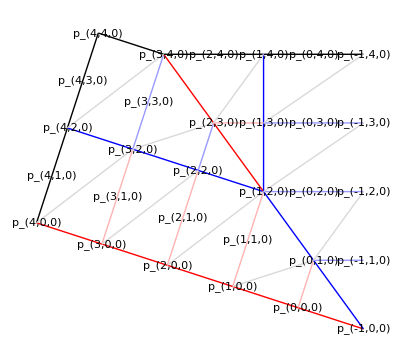

Corresponding points in the folded form have the same subscripts but will have head pp, e.g., pp_(i,j,k). Here are the points of a single sector in 3D.

-Graphics3D-

These aren’t accurate, of course; they’re drawings that are close to the proper vertex positions. The goal of this notebook is to solve for what those vertex positions actually are.

#### FlasherWrapRules[v]

Many of our functions can be applied to both the crease pattern points p_(i,j,k) and folded form points pp_(i,j,k). Those functions will take an argument, v, which represents the symbolic head, e.g., p or pp.

FlasherWrapRules[v] returns a rule that maps points with index i=–1 to the appropriate points in the adjacent sector.

```mathematica
FlasherWrapRules[v_]:=Subscript[v, -1,j_,k_]:>Subscript[v, j,0,k-1]
```

#### FlasherDefaultCPRules[p, m]

FlasherDefaultCPRules[p, m] returns a rule that maps any 2D vertex p_(i, j, k) to its theoretically ideal position in the CP for rotational order m.

```mathematica
FlasherDefaultCPRules[p_,m_]:={Subscript[p, i_,j_,k_]:>FlasherRotation2D[k,m].N[1/2{Cot[π/m],1}+If[i+1≥j,(i+1) U[π/2+(2π)/m]+Tan[π/m]j U[(2π)/m],j U[π/2]-Tan[π/m](i+1)U[0]]]}
```

Example.

```mathematica
Module[{},
FlasherDefaultCPRules[p,4]
]//ShowExample
```

Example: central polygon.

```mathematica
Module[{},
Subscript[p, 0,0,0]/.FlasherDefaultCPRules[p,4]
]//ShowExample
```

### Fold lines and labeled vertices

#### Notes

This section constructs portions of flashers in 2D (crease pattern, CP) and 3D (folded form, FF).

Fold lines are also used to extract the isometry lines.

#### FlasherBorderFold FlasherSharpFold[f] FlasherMedFold[f] FlasherLightFold

Color-coding for crease types. There are three weights of creases, each of which may come in either mountain or valley parity. We'll make functions that return the color for each type.

FlasherBorderFold is the border of the pattern.

```mathematica
FlasherBorderFold:=Black
```

FlasherSharpFold[f] is the color for a sharp fold, one that is around 180°. The type (signified by hue) is set by the parity variable f: even = valley (red), odd = mountain (blue). Sharp folds are darker than the other two flavors.

```mathematica
FlasherSharpFold[f_]:=If[Mod[f,2]==0,RGBColor[1,0,0],RGBColor[0,0,1]]
```

FlasherMedFold[p] is the color for a medium fold, one that is around 90°. As with FlasherSharpFold[], the type (signified by hue) is set by the parity variable p. Medium folds are lighter than sharp folds.

```mathematica
FlasherMedFold[f_]:=If[Mod[f,2]==0,RGBColor[1,.7,.7],RGBColor[.6,.6,1]]
```

FlasherLightFold is the color for a light fold, one that is around 0° (a slight bend). Since the direction of a light fold is not generally known, we do not give it a type and we use light gray for the color.

```mathematica
FlasherLightFold := GrayLevel[.85]
```

#### FlasherVertexLabel[u, v_(i,j,k)] FlasherFirstSectorAllVerticesLabels[u, v, n]

We’ll construct a parameterized representation of the fold pattern for a single sector that describes the structure of both the crease pattern and the folded form. Three parameters characterize the structure topologically: {r, h, m}, where r is the number of “rings” (basically, the number of up-and-down layers), h is the height order (the number of basic panels in each up-and-down layer), and m is the rotational symmetry. For sector-specific functions, k is the rotational index of the particular sector.

First, some labels so we know what we’re looking at.

FlasherVertexLabel[u, v_(i,j,k)] takes a subscripted point and returns a label at its position, using character u. Note that the subscripts are given exactly as passed, but we apply index wrap-around to the position vector.

```mathematica
FlasherVertexLabel[u_,Subscript[v_, i_,j_,k_]]:=Text[Subscript[Style[u,Bold], i,j,k],Subscript[v, i,j,k]/.FlasherWrapRules[v]]
```

Example

```mathematica
Module[{},
FlasherVertexLabel["p",Subscript[p, 0,0,0]]
]//ShowExample
```

Example, showing wrap-around.

```mathematica
Module[{},
FlasherVertexLabel["p",Subscript[p, -1,2,4]]
]//ShowExample
```

FlasherFirstSectorAllVerticesLabels[u, v, n] returns a set of labels for all points in the first (k=0) sector up to the nth ring, using u_(i,j,k) (where u is a string) to represent point v_(i,j,k).

Note that this displays all possible vertices, even those that fall in the middle of a panel line (which is the case for h≥2).

```mathematica
FlasherFirstSectorAllVerticesLabels[u_,v_,n_]:=Style[Table[FlasherVertexLabel[u,Subscript[v, i,j,0]],{i,-1,n},{j,0,n}],Black]
```

Example.

```mathematica
Module[{n=3,m=5},Graphics[FlasherFirstSectorAllVerticesLabels["p",p,n]/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

#### FlasherSectorQuads[v, r, h, k] FlasherSectorTriangles[v, r, h, k]

FlasherSectorQuads[v, r, h, k] returns a list of vertex quadruplets for the quadrilateral facets in this order:
	bottom-outside
	bottom-inside
	top-inside
	top-outside
So that in the major region, the vertices cycle counterclockwise and in the minor region they cycle clockwise.

The quads will need to be triangulated; each quad can be triangulated in two ways.

```mathematica
FlasherSectorQuads[v_,r_,h_,k_]:=Module[{n,i,j,quad},
n=r*h;(* total number of radial increments *)
Flatten[{
(* major region *)
Table[{j=h*ig;
If[Min[j+h,i]>j,quad[Subscript[v, i,j,k],Subscript[v, i-1,j,k],Subscript[v, i-1,Min[j+h,i],k],Subscript[v, i,Min[j+h,i+1],k]],{}]
},{ig,0,r-1},{i,h*ig,n}],
(* minor region *)
Table[{i=h*ig-1;
If[Min[i+h,j-2]>i,quad[Subscript[v, i,j,k],Subscript[v, i,j-1,k],Subscript[v, Min[i+h,j-2],j-1,k],Subscript[v, Min[i+h,j-1],j,k]],{}]
},{ig,0,r-1},{j,h*ig+1,n}]
}]/.quad->List/.FlasherWrapRules[v]]
```

Example. Display and number the quads.

```mathematica
Module[{r=3,h=2,m=5,fsq,fspolys},
fsq=FlasherSectorQuads[p,r,h,0];
fspolys=MapIndexed[With[{ctr=Plus@@#1/4},{Style[Polygon[ctr+0.8(#1-ctr)],LightGray],Style[Text["q"<>ToString[#2⟦1⟧],ctr],Darker[Green]]}]&,fsq];
Graphics[{fspolys,FlasherFirstSectorAllVerticesLabels["p",p,r*h]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

FlasherSectorTriangles[v, r, h, k] returns a list of vertex triplets for the triangle facets in this order:
	bottom-outside
	bottom-inside
	top-inside
	top-outside
So that in the major region, the vertices cycle counterclockwise and in the minor region they cycle clockwise.

Note that we build this function by duplicating the quad function and editing slightly. When the strict inequalities of the latter reach equality (the former), we get a triangle.

```mathematica
FlasherSectorTriangles[v_,r_,h_,k_]:=Module[{n,i,j,quad},
n=r*h;(* total number of radial increments *)
Flatten[{
(* major region *)
Table[{j=h*ig;
If[Min[j+h,i]==j,quad[Subscript[v, i,j,k],Subscript[v, i-1,j,k],Subscript[v, i,Min[j+h,i+1],k]],{}]
},{ig,0,r-1},{i,h*ig,n}],
(* minor region *)
Table[{i=h*ig-1;
If[Min[i+h,j-2]==i,quad[Subscript[v, i,j,k],Subscript[v, i,j-1,k],Subscript[v, Min[i+h,j-1],j,k]],{}]
},{ig,0,r-1},{j,h*ig+1,n}]
}]/.quad->List/.FlasherWrapRules[v]]
```

Example. Display and number the triangles.

```mathematica
Module[{r=3,h=2,m=5,fsq,fspolys},
fsq=FlasherSectorTriangles[p,r,h,0];
fspolys=MapIndexed[With[{ctr=Plus@@#1/3},{Style[Polygon[ctr+0.8(#1-ctr)],LightGray],Style[Text["q"<>ToString[#2⟦1⟧],ctr],Darker[Green]]}]&,fsq];
Graphics[{fspolys,FlasherFirstSectorAllVerticesLabels["p",p,r*h]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

#### FlasherSectorFoldedFoldLines[v, r, h, k] FlasherSectorDiagFoldLinesX[v, r, h, k] FlasherSectorDiagFoldLinesY[v, r, h, k] FlasherSectorDiagFoldLinesZ[v, r, h, k] FlasherSectorFoldLines[v, r, h, k, opts] (options) FlasherSectorDiagFoldLines

FlasherSectorFoldedFoldLines[v, r, h, k] returns a list of styled fold lines for the sharp and medium folds, but doesn’t include any if the diagonal folds that cross quads that are only slightly folded.

```mathematica
FlasherSectorFoldedFoldLines[v_,r_,h_,k_]:=Module[{n,i,j},
n=r*h;(* total number of radial increments *)
Flatten[{
(* major region *)
Table[{j=h*ig;
Style[Line[{Subscript[v, i,j,k],Subscript[v, i-1,j,k]}],FlasherSharpFold[ig]],(* bottom of quadrant *)
Style[Line[{Subscript[v, i,j,k],Subscript[v, i,Min[j+h,i+1],k]}],If[i==n,FlasherBorderFold,FlasherMedFold[ig]]](* left of quadrant *)
},{ig,0,r-1},{i,h*ig,n}],
Style[Line[{Subscript[v, n,h*r,k],Subscript[v, n-1,h*r,k]}],FlasherBorderFold],(* extra segment at corner *)
(* diagonal *)
Table[{i=h*ig+j;
Style[Line[{Subscript[v, i-1,i,k],Subscript[v, i,i+1,k]}],FlasherSharpFold[ig+1]]
},{ig,0,r-1},{j,0,h-1}],
(* minor region *)
Table[{i=h*ig-1;
If[ig≠0,Style[Line[{Subscript[v, i,j,k],Subscript[v, i,j-1,k]}],FlasherSharpFold[ig]],{}],(* bottom of quadrant *)
Style[Line[{Subscript[v, i,j,k],Subscript[v, Min[i+h,j-1],j,k]}],If[j==n,FlasherBorderFold,FlasherMedFold[ig+1]]](* left of quadrant *)
},{ig,0,r-1},{j,h*ig+1,n}]
}]/.FlasherWrapRules[v]]
```

Example.

```mathematica
Module[{r=3,h=2,n,m=5,k=0},
n=r*h;
Graphics[{
FlasherSectorFoldedFoldLines[p,r,h,k],
FlasherFirstSectorAllVerticesLabels["p",p,n]
}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

There are two ways to triangulate each quad, of course, so there are many ways to create the diagonals (and the different ways set which direction each panel flexes in the folded form and/or during deployment). We give a few possible algorithms.

FlasherSectorDiagFoldLinesX[v, r, h, k] returns a list of the diagonal folds that cross each quad.

This is the original arrangement of the diagonal folds that I used in my initial analysis for LLNL. Note that the way I construct this pattern relies on the order that the quads were built.

```mathematica
FlasherSectorDiagFoldLinesX[v_,r_,h_,k_]:=Module[{fsq,nmajor,nminor,qmajor,qminor,qrmajor,qrminor,n},
fsq=FlasherSectorQuads[v,r,h,k];
nmajor=(Length[fsq]+r)/2;(* number in first row of major region *)
nminor=nmajor-r;(* number in first row of minor region *)
qmajor=Take[fsq,nmajor];(* the major quads *)
qminor=Take[fsq,-nminor];(* the minor quads *)
(* now partition into individual rows *)
qrmajor = {};n=r*h;(* number of elements in major row *)
While[n>0,AppendTo[qrmajor,Take[qmajor,n]];qmajor=Drop[qmajor,n];n-=h];
qrminor={};n=r*h-1;(* number of elements in 1st minor row *)
While[n>0,AppendTo[qrminor,Take[qminor,n]];qminor=Drop[qminor,n];n-=h];
Flatten[Join[MapIndexed[Style[Line[If[Mod[#2⟦2⟧+(h-1)*(#2⟦1⟧-1)+1,2]==0,#1⟦{1,3}⟧,#1⟦{2,4}⟧]],FlasherLightFold]&,qrminor,{2}],
MapIndexed[Style[Line[If[Mod[#2⟦2⟧+(h-1)*(#2⟦1⟧-1)+1,2]==0,#1⟦{1,3}⟧,#1⟦{2,4}⟧]],FlasherLightFold]&,qrmajor,{2}]]]/.FlasherWrapRules[v]]
```

Example.

```mathematica
Module[{r=4,h=1,n,m=5,k=0},
n=r*h;
Graphics[{
FlasherSectorFoldedFoldLines[p,r,h,k],
FlasherSectorDiagFoldLinesX[p,r,h,k],
FlasherFirstSectorAllVerticesLabels["p",p,n]
}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

FlasherSectorDiagFoldLinesY[v, r, h, k] returns a list of the diagonal folds that cross each quad.

This assignment is consistent relative to the quad position and splits the obtuse angles and, because of its consistent direction, insures that there are never any interior degree-4 vertices. This is the method used in the Zirbel flasher paper.

```mathematica
FlasherSectorDiagFoldLinesY[v_,r_,h_,k_]:=Module[{fsq},
fsq=FlasherSectorQuads[v,r,h,k];
Style[Line[#⟦{1,3}⟧],FlasherLightFold]&/@fsq/.FlasherWrapRules[v]]
```

Example

```mathematica
Module[{r=4,h=1,n,m=5,k=0},
n=r*h;
Graphics[{
FlasherSectorFoldedFoldLines[p,r,h,k],
FlasherSectorDiagFoldLinesY[p,r,h,k],
FlasherFirstSectorAllVerticesLabels["p",p,n]
}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

FlasherSectorDiagFoldLinesZ[v, r, h, k] returns a list of the diagonal folds that cross each quad.

This assignment is consistent relative to the quad position and splits the quads in the opposite direction from Y, which seems to be the direction that the pattern naturally flexes in the partially folded state.

```mathematica
FlasherSectorDiagFoldLinesZ[v_,r_,h_,k_]:=Module[{fsq},
fsq=FlasherSectorQuads[v,r,h,k];
Style[Line[#⟦{2,4}⟧],FlasherLightFold]&/@fsq/.FlasherWrapRules[v]]
```

Example.

```mathematica
Module[{r=4,h=1,n,m=5,k=0},
n=r*h;
Graphics[{
FlasherSectorFoldedFoldLines[p,r,h,k],
FlasherSectorDiagFoldLinesZ[p,r,h,k],
FlasherFirstSectorAllVerticesLabels["p",p,n]
}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

FlasherSectorFoldLines[v, r, h, k, opts] returns a flat list of both folded fold lines and diagonal bend lines.

Arguments:
	v — the symbolic head of the points variable
	h — the discrete height of the pattern
	k — the rotation order of the sector.

Options:
	FlasherSectorDiagFoldLines → f, the function to use for diagonal fold lines.

Returns: a list of styled fold lines for the specified sector.

```mathematica
FlasherSectorDiagFoldLines::usage="FlasherSectorDiagFoldLines is an option to FlasherSectorFoldLines that specifies which set of diagonal folds to use in the pattern.";
```

```mathematica
Options[FlasherSectorFoldLines]={
FlasherSectorDiagFoldLines->FlasherSectorDiagFoldLinesY
};
```

```mathematica
FlasherSectorFoldLines[v_,r_,h_,k_,opts___]:=Module[{fsdfl},
fsdfl=FlasherSectorDiagFoldLines/.{opts}/.Options[FlasherSectorFoldLines];
Join[FlasherSectorFoldedFoldLines[v,r,h,k],fsdfl[v,r,h,k]]]
```

Example, default diagonals.

```mathematica
Module[{r=4,h=1,n,m=5,k=0},
n=r*h;
Graphics[{FlasherSectorFoldLines[p,r,h,k],
FlasherFirstSectorAllVerticesLabels["p",p,n]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

Example, diagonals going the opposite direction.

```mathematica
Module[{r=4,h=1,n,m=5,k=0},
n=r*h;
Graphics[{FlasherSectorFoldLines[p,r,h,k,FlasherSectorDiagFoldLines->FlasherSectorDiagFoldLinesZ],
FlasherFirstSectorAllVerticesLabels["p",p,n]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

#### FlasherFirstSectorVertices[v, r, h] FlasherFirstSectorVerticesDistinct[v, r, h]

FlasherFirstSectorVertices[v, r, h] returns a list of all of the vertex variables of type v that appear as vertices in the first sector of the specified FlasherLines pattern.

These are used to generate a labeled graphical representation of the first sector.

```mathematica
FlasherFirstSectorVertices[v_,r_,h_]:=Union[Cases[{FlasherSectorFoldLines[v,r,h,0]},Subscript[v, ___],∞]]
```

Example

```mathematica
Module[{r=2,h=2},
FlasherFirstSectorVertices[p,r,h]
]//ShowExample
```

Example: same sector as above, but only label the vertices that actually appear in the pattern. Left is all possible vertices; right is FlasherFirstSectorVertices.

```mathematica
Module[{r=2,h=2,n,m=5},
n=r h;
GraphicsRow[{Graphics[{FlasherSectorFoldLines[p,r,h,0],FlasherFirstSectorAllVerticesLabels["p",p,n]}],Graphics[{FlasherSectorFoldLines[p,r,h,0],FlasherVertexLabel["p",#]&/@FlasherFirstSectorVertices[p,r,h]}]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

When it comes time to set constraints, we’ll want to consider only those vertices that are uniquely associated with the first sector.

FlasherFirstSectorVerticesDistinct[v, r, h] returns just those vertices whose third index is zero.

These are used to get the variables for the optimization.

```mathematica
FlasherFirstSectorVerticesDistinct[v_,r_,h_]:=Union[Cases[{FlasherSectorFoldLines[v,r,h,0]},Subscript[v, _,_,0],∞]]
```

Example

```mathematica
Module[{r=2,h=2},
FlasherFirstSectorVerticesDistinct[p,r,h]
]//ShowExample
```

Example.

```mathematica
Module[{r=2,h=2,n,m=5},
n=r h;
GraphicsRow[{Graphics[{FlasherSectorFoldLines[p,r,h,0],FlasherFirstSectorAllVerticesLabels["p",p,n]}],Graphics[{FlasherSectorFoldLines[p,r,h,0],FlasherVertexLabel["p",#]&/@FlasherFirstSectorVerticesDistinct[p,r,h]}]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

#### FlasherOuterRingSectorVertices[v, r, h, m, k]

FlasherOuterRingSectorVertices[v, r, h, m, k] returns the vertices of the outer ring of the kth sector. Useful for both the FlasherOuterRingFns (where v→pp, see next) and for finding incircle and circumcircle of crease patterns (where v→p).

```mathematica
FlasherOuterRingSectorVertices[v_,r_,h_,m_,k_] :=Join[Table[Subscript[v, r*h,j*h,k],{j,0,r}],Table[Subscript[v, i*h-1,r*h,k],{i,r}]]
```

Example

```mathematica
Module[{r=3,h=3},
FlasherOuterRingSectorVertices[p,r,h,5,0]
]//ShowExample
```

#### FlasherLabeledSector[u, v, r, h, m, opts] (options) FlasherSectorDiagFoldLines FlasherLines[v, r, h, m, opts] (options) FlasherSectorDiagFoldLines

FlasherLabeledSector[u, v, r, h, m, opts] gives labeled points and lines of the first sector of a flasher, parameterized on the vertices.

```mathematica
FlasherLabeledSector[u_,v_,r_,h_,m_,opts___]:={FlasherSectorFoldLines[v,r,h,0,opts],FlasherVertexLabel[u,#]&/@FlasherFirstSectorVertices[v,r,h]}
```

Example

```mathematica
Module[{r=2,h=2,m=5},
Graphics[{FlasherLabeledSector["p",p,r,h,m]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

FlasherLines[v, r, h, m] returns the line pattern for the full flasher of rotational order m.

```mathematica
FlasherLines[v_, r_,h_,m_,opts___]:=Table[FlasherSectorFoldLines[v,r,h,k,opts],{k,0,m-1}]
```

Example

```mathematica
Module[{r=2,h=2,m=5},
Graphics[{FlasherLines[p,r,h,m]}/.FlasherDefaultCPRules[p,m]]
]//ShowExample
```

### Folded form

#### FlasherFFPointRotation[i, j] FlasherFFPointRadialOffset[i, j] FlasherFFPointDiscreteHeight[i, j, h]

The points of a single sector of the pattern have two indices, i and j. There are a couple of useful functions of these indices that are used to compute the ideal folded form position.

FlasherFFPointRotation[i, j] gives the number of times a point in the CP gets rotated in the folded form.

```mathematica
FlasherFFPointRotation[i_,j_]:=If[j≤i+1,i+1,j]
```

Example. Show this for a sector.

```mathematica
Module[{},Graphics[Table[Text[{i,j}->FlasherFFPointRotation[i,j],{-i,j}],{i,0,4},{j,0,4}]]
]//ShowExample
```

FlasherFFPointRadialOffset[i,j] gives the (dimensionless) desired radial displacement in the folded form. This will ultimately be scaled by dr (and some trig stuff).

```mathematica
FlasherFFPointRadialOffset[i_,j_]:=If[j≤i+1,i(i+1)+j,j(j+1)-(i+1)]
```

Example. Show this for a sector.

```mathematica
Module[{},Graphics[Table[Text[{i,j}->FlasherFFPointRadialOffset[i,j],{-i,j}],{i,0,4},{j,0,4}]]
]//ShowExample
```

FlasherFFPointDiscreteHeight[i, j, h] returns the discrete height of folded form point pp_(i, j, k) for panel height parameter h.

```mathematica
FlasherFFPointDiscreteHeight[i_,j_,h_]:=Abs[Mod[Min[i+1,j]-h,2h,0]-h]
```

Example. Show this for a sector of height 2.

```mathematica
Module[{},
Graphics[Table[Text[{i,j}->FlasherFFPointDiscreteHeight[i,j,2],{-i,j}],{i,0,4},{j,0,4}]]
]//ShowExample
```

#### FlasherDefaultFFRules[pp, h, m, dr]

FlasherDefaultFFRules[pp, h, m, dr] returns a set of rules giving 3-dimensional coordinates for the points of the folded form for height order h, rotational order m, with dr being the radial spacing of the concentric layers within a given horizontal plane relative to the radial distance of the innermost vertex (central polygon). This is an idealized structure, and in general will not be isometric to a flat crease pattern. But we’ll use it as a starting point when we solve for the crease pattern.

```mathematica
FlasherDefaultFFRules[pp_,h_,m_,dr_:.1]:={Subscript[pp, i_,j_,k_]:>N[FlasherRotation3D[k+FlasherFFPointRotation[i,j],m].(1/2(1+dr FlasherFFPointRadialOffset[i,j]/h){Cot[π/m],1,0}+{0,0, FlasherFFPointDiscreteHeight[i,j,h]Tan[π/m]})]}
```

Example.

```mathematica
Module[{},
FlasherDefaultFFRules[pp,1,4]
]//ShowExample
```

Example: first point in the central polygon.

```mathematica
Module[{},
Subscript[pp, 0,0,0]/.FlasherDefaultFFRules[pp,1,4]
]//ShowExample
```

Example. Graphical representation.

```mathematica
Module[{r=3,h=3,m=4,dr=.01},
Graphics3D[FlasherSectorFoldLines[pp,r,h,0]/.FlasherDefaultFFRules[pp,h,m,dr],Axes->True]
]//ShowExample
```

### Vertices as vectors and scalars

#### Notes

In this section, we set up the constraint functions needed to solve for specific flashers that are isometric to a flat CP. Note that because of rotational symmetry, we only need to consider conditions on vertices in the first sector.

One of the key notions of this section is to distinguish between vertices and scalar variables. The vertices are vector quantities, parameterized as two- and three-subscript expressions p_(i, j, k) and pp_(i, j, k). When we get around to solving for coordinates, we will transform these into scalar variables, which are also subscripted expressions (see FlasherScalarize, next section), but each of these subscripted variables represents a scalar value.

#### FlasherVars[]

FlasherVars[] gives a list of of symbolic variables used for vectors and scalars. We use this only to generate examples. When we set up and solve equations, we’ll use a bespoke list made up of local variables to avoid unintentional collisions in case someone has created other definitions for p, pp, etc.

```mathematica
FlasherVars[]={p,px,py,pp,ppx,ppy,ppz};
```

#### FlasherScalarize[vars, obj, m]

FlasherScalarize[vars, obj, m] takes an object that contains p or pp points and converts three-subscript vertices p_(i, j, k) and pp_(i, j, k) into vectors of components p_(i,j,0)→{px_(i, j), py_(i,j)} and pp_(i,j,0)→{ppx_(i,j), ppy_(i,j), ppz_(i,j)}, respectively. It also applies rotation based on the rotational subscript k for rotational order m (thereby removing subscript k from obj).

Note that we implement wrap-around indexing.

```mathematica
FlasherScalarize[vars_,obj_,m_]:=Module[{p,px,py,pp,ppx,ppy,ppz},
{p,px,py,pp,ppx,ppy,ppz}=vars;
obj/.{FlasherWrapRules[p],FlasherWrapRules[pp]}/.{
Subscript[p, i_,j_,k_]:>FlasherRotation2D[k,m].{Subscript[px, i,j],Subscript[py, i,j]},
Subscript[pp, i_,j_,k_]:>FlasherRotation3D[k,m].{Subscript[ppx, i,j],Subscript[ppy, i,j],Subscript[ppz, i,j]}}]
```

Examples.

```mathematica
Module[{},
FlasherScalarize[FlasherVars[],{Subscript[p, 1,2,0]},4]
]//ShowExample
```

```mathematica
Module[{},
FlasherScalarize[FlasherVars[],{Subscript[pp, 1,2,0],Subscript[pp, 1,2,1],Subscript[pp, -1,2,1]},4]
]//ShowExample
```

#### FlasherDefaultScalarRules[vars, r, h, m, dr]

FlasherDefaultScalarRules[vars, r, h, m, dr] returns a list of rules for all of the scalar variables that are used in a flasher with the given parameters.

Note that while FlasherDefaultCPRules and FlasherDefaultFFRules produced rules that were parameterized on their indices, this returns individual rules for each possible subscripted scalar variable.

```mathematica
FlasherDefaultScalarRules[vars_,r_,h_,m_,dr_]:=Module[{p,px,py,pp,ppx,ppy,ppz,cprules,ffrules,fsv,svars,vals},
{p,px,py,pp,ppx,ppy,ppz}=vars;
cprules=FlasherDefaultCPRules[p,m];
ffrules=FlasherDefaultFFRules[pp,h,m,dr];
fsv=Join[FlasherFirstSectorVerticesDistinct[p,r,h],FlasherFirstSectorVerticesDistinct[pp,r,h]];
svars=Flatten[FlasherScalarize[vars,fsv,m]];
vals=Flatten[fsv/.Join[cprules,ffrules]];
MapThread[#1->#2&,{svars,vals}]]
```

Example.

```mathematica
Module[{vars=FlasherVars[],r=2,h=1,m=4,dr=.01},
FlasherDefaultScalarRules[vars,r,h,m,dr]
]//ShowExample
```

#### FlasherVertexRules[vars, m, srules]

FlasherVertexRules[m, srules] takes a rotational order m and a set of scalar-value rules srules (like the output of FlasherDefaultScalarRules) and returns a set of rules that apply those scalar values to vector vertex coordinates. It’s a way of applying values to un-Scalarized objects, like the graphical representations.

```mathematica
FlasherVertexRules[vars_,m_,srules_]:=Module[{p,px,py,pp,ppx,ppy,ppz},{
{p,px,py,pp,ppx,ppy,ppz}=vars;
Subscript[p, i_,j_,k_]:>(FlasherRotation2D[k,m].{Subscript[px, i,j],Subscript[py, i,j]}/.srules),
Subscript[pp, i_,j_,k_]:>(FlasherRotation3D[k,m].{Subscript[ppx, i,j],Subscript[ppy, i,j],Subscript[ppz, i,j]}/.srules)
}]
```

### Analysis and constraints

#### Notes

The functions in this section generate the equations that we solve to find the CP and FF of a flasher. All equations are given in terms of subscripted scalar variables, e.g., p_(i,j) and pp_(i,j).

#### FlasherCPFns[vars, m]

FlasherCPFns[vars, m] returns a list containing a single function that pins the rotational orientation of the crease pattern to that of the default CP pattern. Specifically, it constrains the vertex p_(0, 0, 0) to lie on a line through the origin that passes through the initial point position.

Note that only a single function is returned, but we wrap it in a list to be parallel with the other functions that return lists of multiple elements.

```mathematica
FlasherCPFns[vars_, m_]:=Module[{p,px,py,pp,ppx,ppy,ppz},
{p,px,py,pp,ppx,ppy,ppz}=vars;
{FlasherScalarize[vars,Subscript[p, 0,0,0],m].FlasherRotation2D[1,4].(Subscript[p, 0,0,0]/.FlasherDefaultCPRules[p,m])}]
```

Example.

```mathematica
Module[{vars=FlasherVars[],r=2,h=1,m=4,dr=.01,cpfns},
cpfns=FlasherCPFns[vars,m];
PrintThis[cpfns];
cpfns/.FlasherDefaultScalarRules[vars,r,h,m,dr]
]//ShowExample
```

#### FlasherIsometryFns[vars, r, h, m, opts] (options) FlasherSectorDiagFoldLines

FlasherIsometryFns[vars, r, h, m] returns a list of functions whose value must be zero when isometry is satisfied: CP length = FF length for each segment.

Options:
	FlasherSectorDiagFoldLines → f, to specify which diagonals are used. Passed through to FlasherSectorFoldLines.

We have one equation for every line in the sector. This includes the default set of quad diagonal folds.

```mathematica
FlasherIsometryFns[vars_,r_,h_,m_,opts___]:=Module[{p,px,py,pp,ppx,ppy,ppz,v,fs,lp,dfn,dp,dpp},
{p,px,py,pp,ppx,ppy,ppz}=vars;
(* first sector of flasher, symbolic variable v *)
fs=FlasherSectorFoldLines[v,r,h,0,opts];
(* all line segment vertex pairs in the first sector *)
lp=First/@Flatten[Cases[fs,Line[_],∞]];
(* distance fn that takes a list of point pairs *)
dfn=Mag[Subtract@@#]&;
(* Scalarize cp pairs and compute length *)
dp=dfn/@N[FlasherScalarize[vars,lp/.v->p,m]];
(* Scalarize ff pairs and compute length^2 *)
dpp=dfn/@N[FlasherScalarize[vars,lp/.v->pp,m]];
(* return difference between lengths *)
dpp-dp]
```

Example. Since our test solution is fairly close to correct, these numbers should all be pretty small.

```mathematica
Module[{r=2,h=1,m=4,dr=.01,vars,ifns,srules},
vars=FlasherVars[];
ifns=FlasherIsometryFns[vars,r,h,m];
srules=FlasherDefaultScalarRules[vars,r,h,m,dr];
ifns/.srules
]//ShowExample
```

#### FlasherXYFns[vars, r, h, m, dr]

FlasherXYFns[vars, r, h, m, dr] returns a list of functions that return zero when the x and y coordinates of the folded form points of the specified flasher are equal to their default values for radial spacing dr.

```mathematica
FlasherXYFns[vars_,r_,h_,m_,dr_]:=Module[{p,px,py,pp,ppx,ppy,ppz,ffrules,fsv,fsvn},
{p,px,py,pp,ppx,ppy,ppz}=vars;
ffrules=FlasherDefaultFFRules[pp,h,m,dr];
fsv=FlasherFirstSectorVerticesDistinct[pp,r,h];(* vertices *)
fsvn=fsv/.ffrules;(* desired values *)
Flatten[Take[#,2]&/@(N[FlasherScalarize[vars,fsv,m]]-fsvn)]]
```

Example. The default values should exactly satisfy these equations.

```mathematica
Module[{r=2,h=1,m=4,dr=.01,vars,xyfns,ffrules},
vars=FlasherVars[];
xyfns=FlasherXYFns[vars,r,h,m,dr];
ffrules=FlasherDefaultFFRules[pp,h,m,dr];
xyfns/.FlasherDefaultScalarRules[vars,r,h,m,dr]
]//ShowExample
```

#### FlasherOuterRingFns[vars, r, h, m, dr, dz]

FlasherOuterRingFns[vars, r, h, m, soln, dz] returns a set of functions that pins the z-values of the outer ring vertices to the values from the solution times a value (1+dz), which lets you nudge the outer ring to be taller or shorter than the default value. This is analogous to the most successful rule set used in my initial analysis. A nice aspect of it is that it always perfectly balances the number of degrees of freedom.

```mathematica
FlasherOuterRingFns[vars_,r_,h_,m_,dr_,dz_:0] :=Module[{p,px,py,pp,ppx,ppy,ppz,verts,ffrules},
{p,px,py,pp,ppx,ppy,ppz}=vars;
verts=FlasherOuterRingSectorVertices[pp,r,h,m,0];
ffrules=FlasherDefaultFFRules[pp,h,m,dr];
Last/@(FlasherScalarize[vars,verts,m]-(1+dz)(verts/.ffrules))]
```

Example.

```mathematica
Module[{r=2,h=1,m=4,dr=.01,dz=.02,vars,ffrules,orfns},
vars=FlasherVars[];
orfns=FlasherOuterRingFns[vars,r,h,m,dr,dz];
PrintThis[orfns];
orfns/.FlasherDefaultScalarRules[vars,r,h,m,dr]
]//ShowExample
```

#### Degrees of freedom analysis.

Here’s a bit of analysis in which we explicitly enumerate the degrees of freedom in our variables and how they are absorbed by the constraint equations.

Here’s an example.

```mathematica
Module[{r=2,h=1,m=4,dr=.1},
GraphicsRow[{
Graphics[FlasherLabeledSector["p",p,r,h,m]],
Graphics[FlasherLines[p,r,h,m]],
Graphics3D[FlasherLabeledSector["pp",pp,r,h,m]],
Graphics3D[FlasherLines[pp,r,h,m]]
}/.Join[FlasherDefaultCPRules[p,m],FlasherDefaultFFRules[pp,h,m,0.1]]]
]//ShowExample
```

Number of distinct vertices in the first sector:

```mathematica
Module[{r=2,h=1,m=4},
Length[FlasherFirstSectorVerticesDistinct[p,r,h]]
]//ShowExample
```

The number of DOF should be a total of 5 times that number; 2 for each vertex in the CP, 3 for each vertex in the FF.

Look at a couple different examples. (You can plug in different numbers for r, h, and m.) Un-Hold the expression to see the results.

```mathematica
Module[{r=3,h=3,m=4,dr=.05,vars,nverts,nisos,nxys,ndwns,norrngs},
vars=FlasherVars[];
Print[GraphicsRow[{
Graphics[FlasherLabeledSector["p",p,r,h,m]],
Graphics[FlasherLines[p,r,h,m]],
Graphics3D[FlasherLabeledSector["pp",pp,r,h,m]],
Graphics3D[FlasherLines[pp,r,h,m]]
}/.Join[FlasherDefaultCPRules[p,m],FlasherDefaultFFRules[pp,h,m,0.1]]]];
nverts=Length[FlasherFirstSectorVerticesDistinct[p,r,h]];
Print["number of vertices = ",nverts];
Print["number of variables = ",5*nverts];
Print["number of CP position constraints = ",1];
nisos=Length[FlasherIsometryFns[vars,r,h,m]];
Print["number of all isometries = ",nisos];
nxys=Length[FlasherXYFns[vars,r,h,m,dr]];
Print["number of xyfns = ",nxys];
norrngs=Length[FlasherOuterRingFns[vars,r,h,m,dr,0]];
Print["number of norrngs = ",norrngs];
Print["Remaining DOF = ",5 * nverts-(1+nisos+nxys+norrngs)];
]//ShowExample
```

### Flasher construction

#### Notes

Here we set up a solution that solves all the relevant equations. You can play with these values to change the design:
	r — the number of rings.
	h — the height order (how many turns a diagonal takes to get from the bottom to the top of a ring)
	m — the rotational symmetry
	dr — the radial spacing of successive vertices in the same plane.
Note that the bottom is not necessarily perfectly flat. Rather, the bottom of the outer ring and the central polygon are both forced to z=0, but the other “down” vertices can (and typically do) take on slightly nonzero values.

If the root-finder fails, the isometry values will be reported. Any values that are not zero (or nearly so) represent an isometry violation between the crease pattern and folded form.

#### FlasherLabeledCPSectorGraphics FlasherLabeledFFSectorGraphics3D FlasherCPGraphics FlasherFFGraphics3D FlasherDetails

```mathematica
FlasherLabeledCPSectorGraphics::usage="FlasherLabeledCPSectorGraphics is a property of a flasher TObj that gives a labeled representation of the first sector of the crease pattern.";
```

```mathematica
FlasherLabeledFFSectorGraphics3D::usage="FlasherLabeledFFSectorGraphics3D is a property of a flasher TObj that gives a labeled representation of the first sector of the folded form.";
```

```mathematica
FlasherCPGraphics::usage="FlasherCPGraphics is a property of a flasher TObj that gives a styled representation of the crease pattern.";
```

```mathematica
FlasherFFGraphics3D::usage="FlasherFFGraphics3D is a property of a flasher TObj that gives a styled representation of the folded form.";
```

```mathematica
FlasherDetails::usage="FlasherDetails is a property of a flasher TObj that gives a list of additional data about the flasher.";
```

#### MakeFlasher[r, h, m, dr] (options) FlasherSectorDiagFoldLines

MakeFlasher[r, h, m, dr] sets up and solves for the design of a flasher.

Arguments:
	r -- the number of rings.
	h -- the height order (how many turns a diagonal takes to get from the bottom to the top of a ring)
	m -- the rotational symmetry
	dr -- the radial spacing of successive vertices in the same plane.

Options:
 	FlasherSectorDiagFoldLines → f, specifies the orientation of the quad diagonal fold lines. Passed through to FlasherSectorFoldLines.
 	TypeMinimumAngle is passed through to ReassignGraph3D.

Returns: a TGraph3DAssigned, with a few additional properties:
	FlasherLabeledCPSectorGraphics — a Graphics of the first sector of the CP with vertex labels
	FlasherLabeledFFSectorGraphics3D — a Graphics3D of the first sector of the FF with vertex labels
	FlasherCPGraphics — a Graphics of the CP with no polygons and color-coded fold lines
	FlasherFFGraphics3D — a Graphics3D of the FF with no polygons and color-coded fold lines
	FlasherDetails — a list of rules giving assorted numerical values.

```mathematica
MakeFlasher::badiso="Warning: isometry equations could not be satisfied. Residual error is `1.`";
```

```mathematica
MakeFlasher[r_,h_,m_,dr_,opts___]:=Module[{vars,p,px,py,pp,ppx,ppy,ppz,dz,eqnfns,srules,allvars,newvars,fwd,bkd,args,soln,vertrules,isovals,cpsg,cplg,ffsg,fflg,picdia,pccdia,cpccdia,orverts,ffverts,oph,opw,cpicdia,ffdia,ffh,cpedges,ffedges,btedges,verts,edges,verts3d,tobj,msgs},

(* PART I: solve for the flasher *)

vars={p,px,py,pp,ppx,ppy,ppz};
eqnfns=Join[
FlasherCPFns[vars,m],
FlasherIsometryFns[vars,r,h,m,opts],
FlasherXYFns[vars,r,h,m,dr],
FlasherOuterRingFns[vars,r,h,m,dr,dz],(* dz is now a variable *)
{Subscript[ppz, 0,0]}(* forces central polygon to z=0 *)
];
srules=Append[FlasherDefaultScalarRules[vars,r,h,m,dr],dz->0];allvars=First/@srules;
newvars=Table[Unique[],{Length[allvars]}];fwd=MapThread[#1->#2&,{allvars,newvars}];bkd=MapThread[#2->#1&,{allvars,newvars}];args={eqnfns/.fwd,Transpose[{newvars,allvars/.srules}]};
soln=Check[(FindRoot@@args),Abort[],{}];
soln = soln /. bkd;
vertrules=FlasherVertexRules[vars,m,soln];
isovals=Abs/@FlasherIsometryFns[vars,r,h,m,opts]/.soln;
If[Plus@@isovals>10^-6,Message[MakeFlasher::badiso,isovals]];

(* PART II: compute graphical bits and diagnostic info *)

(* graphical images, sector & pattern, cp & ff *)
cpsg=Graphics[FlasherLabeledSector["p",p,r,h,m,opts]]/.vertrules;
cplg=Graphics[FlasherLines[p,r,h,m,opts]]/.vertrules;
ffsg=Graphics[FlasherLabeledSector["pp",pp,r,h,m,opts]]/.vertrules;
fflg=Graphics[FlasherLines[pp,r,h,m,opts]]/.vertrules;
(* central polygon incircle diameter *)
picdia=1;
(* central polygon circumcircle diameter *)
pccdia=2*Mag[Subscript[p, 0,0,0]/.vertrules];
(* cp outermost vertices *)
orverts=FlasherOuterRingSectorVertices[p,r,h,m,0]/.vertrules;
(* crease pattern incircle diameter *)
cpicdia=2*Min[Mag/@orverts];
(* crease pattern circumcircle diameter *)
cpccdia=2*Max[Mag/@(orverts/.vertrules)];
(* outermost panel height *)
oph=Mag[(Subscript[p, r*h,r*h,0]-Subscript[p, r*h,(r-1)*h,0])/.vertrules];
(* outermost panel width *)
opw=Mag[(Subscript[p, r*h,r*h,0]-Subscript[p, r*h-1,r*h,0])/.vertrules];
(* outermost vertices in ff *)
ffverts=FlasherFirstSectorVerticesDistinct[pp,r,h]/.vertrules;
(* folded form circumcircle diameter *)
ffdia=2*Max[Mag/@Take[#,2]&/@ffverts];
(* folded form height *)
ffh=Max[Last/@ffverts]-Min[Last/@ffverts];

(* PART III: construct a TGraph3DAssigned *)

(* lists of point pairs for both cp and ff *)
cpedges=First/@Cases[FlasherLines[p,r,h,m,opts],_Line,{0,∞}]/.vertrules;
ffedges=First/@Cases[FlasherLines[pp,r,h,m,opts],_Line,{0,∞}]/.vertrules;
(* ordered 5-tuples, for indexification *)
btedges=MapThread[Join,{cpedges,ffedges},2];
{verts,edges}=Indexify[btedges,2];
verts3d=Take[#,-3]&/@verts;
verts=Take[#,2]&/@verts;
tobj=MakeTGraph[verts,edges]//AddTPlaneGraph//AddTGraph3D[verts3d]//RecalcFoldAngles//ReassignGraph3D[#,opts]&;
(* add the additional properties *)
tobj//AddProperties[{
FlasherLabeledCPSectorGraphics->cpsg,
FlasherLabeledFFSectorGraphics3D->ffsg,
FlasherCPGraphics->cplg,
FlasherFFGraphics3D->fflg,
 FlasherDetails->{
"central polygon incircle diameter"->picdia,
"central polygon circumcircle diameter"->pccdia,
"crease pattern incircle diameter"->cpicdia;
"crease pattern circumcircle diameter"->cpccdia,
"crease pattern incircle diameter"->cpicdia,
"folded form circumcircle diameter"->ffdia,
"outermost panel height"->oph,
"outermost panel width"->opw
}}]]
```

Examples.

```mathematica
Module[{r=2,h=2,m=4,dr=.05,tobj},
tobj=MakeFlasher[r,h,m,dr,TypeMinimumAngle->10.°];
Print[tobj[FlasherDetails]//ColumnForm];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

Another example, with different diagonal folds.

```mathematica
Module[{r=2,h=2,m=5,dr=.1,tobj},
tobj=MakeFlasher[r,h,m,dr,FlasherSectorDiagFoldLines->FlasherSectorDiagFoldLinesZ, TypeMinimumAngle->10.°];
Print[tobj[FlasherDetails]//ColumnForm];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]
]//ShowExample
```

#### HexFlasherGraph3DAssigned

HexFlasherGraph3DAssigned gives a hexagonal version of a flasher.

```mathematica
Clear[HexFlasherGraph3DAssigned];
AddTGraphExample[HexFlasherGraph3DAssigned,
Module[{r=2,h=2,m=6,dr=.05},
MakeFlasher[r,h,m,dr,FlasherSectorDiagFoldLines->FlasherSectorDiagFoldLinesZ, TypeMinimumAngle->10.°]]];
```

Example.

```mathematica
Module[{tobj},
tobj=HexFlasherGraph3DAssigned;
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}/.OrigamiStyle[]]]//ShowExample
```

## Laser scoring

#### Notes

These functions support various forms of laser-scoring. The simplest form of output for laser scoring is to export the Graphics object while applying ScoringStyle[]. This will produce single linear cuts for all fold lines and the border, in different colors, so that one can set different power levels.

Note that we must add the option PlotRangePadding→0 to Graphics objects when we export them so that Mathematica doesn’t add an additional border and down-size the image from the specified dimensions.

### Perforated scoring

#### Notes

One can laser-score patterns in two ways: you can partially ablate fold lines to weaken the paper along the folds, but that requires very good control over power and uniformity. A more forgiving technique is to perforate fold lines. Since the perforation punches all the way through the paper, it’s relatively less sensitive to variation in power level. When we perforate a pattern, though, there are a few tweaks we’d like to make:
	(1) Leave gaps at the ends of lines, to avoid holes precisely at vertices (which creates tear nucleation sites)
	(2) Vary the dashing pattern of perforation, depending on the materials.
Because different laser cutters provide varying level of support for precise perforations, our strategy is to preprocess all of the perforation, fracturing lines into many tiny segments to create the perforation.

The function in this section takes a TGraph+TAssigned, representing a styled crease pattern, and exports a scaled perforated pattern that can be imported into the program that drives the laser cutter (e.g., Corel Draw).

#### ExportPerforatedScoring[file, tobj, opts] (checked class) TGraph, TAssigned (options) ImageWidth, ImageHeight, GapLength, DashPattern, ScoreLineThickness, ShowProgress

ExportPerforatedScoring[file, tobj, opts] takes a TGraph+TAssigned and exports a perforated scoring pattern of the crease pattern  of size imagesize to  file (typically EPS). Options are as follows (all distances in points):
	ImageWidth → w, where w is the desired image width.
	ImageHeight → h, where h is the desired image height. You must supply either width or height (if you specify both, ImageWidth wins out).
	GapLength → d, length of gaps to leave at ends of peforated lines. See Gapify.
	DashPattern → pat, the dashing pattern to use for perforation. See Dashify.
	ScoreLineThickness → t, the desired thickness to use for scoring lines.
	ShowProgress → True | False, whether to display detailed size and the perforated image.

```mathematica
ImageWidth::usage="ImageWidth is an option to ExportPerforatedScoring that specifies the desired width of the score pattern.";
```

```mathematica
ImageHeight::usage="ImageHeight is an option to ExportPerforatedScoring that specifies the desired height of the score pattern.";
```

```mathematica
Options[ExportPerforatedScoring]={
ImageWidth->None,
ImageHeight->None,
GapLength->1.5,
DashPattern->{{1.7,False},{0.3,True}},
ScoreLineThickness->0.216,
ShowProgress->False
};
```

```mathematica
ExportPerforatedScoring::badsize="You must specify either ImageWidth or ImageHeight.";
```

```mathematica
ExportPerforatedScoring[file_String, tobj_TObj,opts___]:=Module[{iw,ih,gl,dp,sp,slt,cp,scale,w,h,g},
AssertClasses[tobj,{TGraph,TAssigned},ExportPerforatedScoring];
iw=ImageWidth/.{opts}/.Options[ExportPerforatedScoring];
ih=ImageHeight/.{opts}/.Options[ExportPerforatedScoring];
gl=GapLength/.{opts}/.Options[ExportPerforatedScoring];
dp=DashPattern/.{opts}/.Options[ExportPerforatedScoring];
sp=ShowProgress/.{opts}/.Options[ExportPerforatedScoring];
slt=ScoreLineThickness/.{opts}/.Options[ExportPerforatedScoring];
cp=CreasePatternGraphics[tobj];
{w,h}=GraphicsExtent[cp];
If[!(iw===None),scale=iw/w;ih=scale h,
If[!(ih===None),scale=ih/h;iw=scale w,
Message[ExportPerforatedScoring::badsize];Abort[]]];
cp=ScaleLines[cp,scale];
If[sp,
Print["width = ",iw," pt, ", iw/28.35," cm, ",iw/72.," in"];
Print["height = ",ih," pt, ",ih/28.35," cm, ",ih/72.," in"];
];
g=Graphics[ExtractFracturedStyledLines[cp]];
g=GapifyByStyle[g,{ValleyLine,MountainLine},GapLength->gl];
g=DashifyByStyle[g,{ValleyLine,MountainLine},DashPattern->dp];
If[sp,
Print[Show[g/.ScoringStyle[ScoreLineThickness->1],Frame->True]];
];
Export[file,Show[g/.ScoringStyle[ScoreLineThickness->slt],PlotRangePadding->0],ImageSize->{iw, ih}]]
```

Example. Show progress, displaying the dimensions and perforated image.

```mathematica
Module[{verts,edges,faces,types,tobj},
verts={{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{3,1}};
edges={{1,2},{2,3},{3,4},{5,6},{6,7},{7,8},{1,5},{2,6},{3,7},{4,8}};
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7}};
types={B,B,B,B,B,B,B,M,V,B};
tobj=MakeTGraphAssigned[verts,edges,faces,types];
Print[CreasePatternGraphics[tobj]/.OrigamiStyle[]];
ExportPerforatedScoring[ExamplesDir[]<>"ExportPerforatedScoring.eps",tobj,ImageHeight->72 (* 1 in *),ShowProgress->True]
]//ShowExample
```

### Veneer scoring

#### Notes

The functions in this section are used to create a laser scoring pattern for veneer+blocking layer laminate, e.g., wood veneer with a foil backing. For such a laminate, with a CO_2 laser, you can set the power to cut through the wood but not the foil or anything underneath it). We create hairline cut lines for border and mountain folds, but for valley folds, we need to leave a kerf, whose width is chosen based on the material thickness and the fold angle.

Kerfs can be created by setting the line width to something wider than a hairline, but if you do this with some (all?) laser cutters, they will render it using “carve” mode, which raster-scans the image as a bitmap. This is very inefficient since the fill factor is so low. So the functions VeneerMultiline and VeneerScoringGraphics render kerfed lines as a series of closely-spaced hairlines, with the number and position of the lines determined from the desired absolute line width and parameters that are characteristic of a given laser cutter. Default values match my own cutter, but you can override the defaults through options.

There is an additional issue to contend with, which is how to treat the line ends. If we simply square off the ends, then when two multilines meet at a vertex, there is a small region of overlap, which can result in scorching or burn-through at the foil. To avoid this, we would like to bevel the ends of a multiline, so that when two multilines meet, there is no overlap between them.

Similarly, when a regular cut line (mountain or border line) meets a (valley) multiline, we should pull back the regular line from the end, since the multiline will have already blown away the material where the endpoints of the multiline meet the cut line.

When it comes to scoring a full crease pattern into veneer, we would like to convert the valley folds to multilines based on their fold angle (larger fold angles need wider kerfs). In order to avoid burn-through, we bevel the ends of the valley fold multilines. The bevel angles depend on the desired thicknesses of the single or multilines of adjacent folds. All this gets sorted out in the function VeneerScoringGraphics.

#### VeneerMultiline[{va, vb}, thickness, spacing] VeneerMultiline[{va, vb}, thickness, spacing, {{α_(a,r),α_(a,l)},{α_(b,r),α_(b,l)}}]

VeneerMultiline[{va, vb}, thickness, spacing] simulates a line segment of thickness thickness, running from va to vb, by returning a list of line segments spaced spacing (or less) apart laterally. This is used to create kerfs using cut-lines (rather than raster-scanned carved patterns). Adjacent lines alternate in direction, so that vector-drawing will be done efficiently, going back and forth.

```mathematica
VeneerMultiline[{va_,vb_},thickness_,spacing_]:=Module[{n,sp,xv},
n=Ceiling[thickness/spacing]; (* number of divisions *)
If[n==0,
{Line[{va,vb}]},
sp = thickness/n;(* actual spacing to use *)
xv=NormalizeReal[{{0,-1},{1,0}}.(vb-va)];(* transverse unit vector *)
Table[Line[{If[EvenQ[i],va,vb]+(i-n/2)sp xv,If[EvenQ[i],vb,va]+(i-n/2)sp xv}],{i,0,n}]]]
```

Example

```mathematica
Module[{},
Graphics[VeneerMultiline[{{0,0},{1,1}},0.4,0.07],Frame->True]
]//ShowExample
```

VeneerMultiline[{va, vb}, thickness, spacing, {{α_(a,r),α_(a,l)},{α_(b,r),α_(b,l)}}] does the same thing, but also angles the boundaries of the ends of the lines according to the angles {{α_(a,r),α_(a,l)},{α_(b,r),α_(b,l)}} at each end of the line. By suitably choosing the cut-back angle, one can avoid overlapping the multiple cut lines, which reduces burn-through at vertices where several multilines come together. The specified angles are the angles relative to the original line, right and left as one is looking from the line toward the vertex.

Note that the format of the four angles is the same as the elements of the list returned by function EdgeVertexAngles.

```mathematica
VeneerMultiline[{va_,vb_},thickness_,spacing_,{{aar_,aal_},{abr_,abl_}}]:=Module[{n,sp,yv,xv,dx,pa,pb},
n=Ceiling[thickness/spacing]; (* number of divisions between lines *)
If[n==0,
{Line[{va,vb}]},
sp = thickness/n;(* actual spacing to use *)
yv=NormalizeReal[vb-va];(* unit vector along the line *)
xv={{0,-1},{1,0}}.yv;(* transverse unit vector *)
Table[
dx=(i-n/2)sp;
pa=va+dx xv+If[i<n/2,-Cot[aal],Cot[aar]]dx yv;
pb=vb+dx xv+If[i<n/2,Cot[abr],-Cot[abl]]dx yv;
Line[{If[EvenQ[i],pa,pb],If[EvenQ[i],pb,pa]}],{i,0,n}]]]
```

Example. A single multiline with distinct angles at each end. We’ll label the angles in this example, to make clear the orientation.

```mathematica
Module[{va,vb},
va={0,0};
vb={1,0};
Graphics[{
Style[Line[{va,vb}],LightGray,AbsoluteThickness[5]],
Style[VeneerMultiline[{va,vb},0.2,0.02,{{22.5°,67.5°},{30°,60°}}],Gray],Style[{Point[va],Text["va",va,{-2,0}]},Red,AbsolutePointSize[5],FontSize->14],
Style[{Point[vb],Text["vb",vb,{2,0}]},Blue,AbsolutePointSize[5],FontSize->14],
Style[{Text["α_(a, r)",{0.2,0.04}],Text["α_(a, l)",{0.1,-0.05}],Text["α_(b, r)",{0.85,-0.04}],Text["α_(b, l)",{0.9,0.05}]},Black,FontSize->16]
},Frame->True]
]//ShowExample
```

And another example, showing four lines converging at a point but cut back so that they don’t overlap.

```mathematica
Module[{},
Graphics[{
VeneerMultiline[{{1,0},{0,0}},0.4,0.05,{{60°,30°},{45°,45°}}],
VeneerMultiline[{{0,1},{0,0}},0.4,0.05,{{60°,30°},{45°,45°}}],
VeneerMultiline[{{-1,0},{0,0}},0.4,0.05,{{60°,30°},{45°,45°}}],
VeneerMultiline[{{0,-1},{0,0}},0.4,0.05,{{60°,30°},{45°,45°}}]
},Frame->True]
]//ShowExample
```

#### VeneerScoringGraphics[tobj, opts] (checked classes) TPlaneGraph, TAssigned (options) ImageWidth, ImageHeight, VeneerThickness, MultilineSpacing, InvertFolds, FoldAngles, ScoreLineThickness

VeneerScoringGraphics[tobj, opts] takes a TPlaneGraph+TAssigned tobj representing the crease pattern and generates a Graphics object that represents a veneer scoring pattern. Border and mountain folds are rendered as hairlines; valley folds are assigned a thickness that specifies the kerf; the kerf is created by making a VeneerMultiline (a group of closely spaced lines). Ends of multilines are angled to avoid overlaps and minimize burn-through at vertices. Options are:
	ImageWidth → w, where w is the desired image width.
	ImageHeight → h, where h is the desired image height. You must supply either width or height (if you specify both, ImageWidth wins out).
	VeneerThickness → vt, where vt is the veneer thickness, also given in points (for unit consistency).
	MultilineSpacing → ls, where ls is the spacing to use in the VeneerMultiline function.
	InvertFolds → True | False inverts the crease assignment in the pattern.
	FoldAngles → angle | anglelist | Automatic, where:
		angle is a single angle used for all valley folds;
		 anglelist is a list of specified angles, one for each edge of the graph;
		 Automatic uses the angles in the FoldAngles property, if it exists, and if not, makes all valley folds 180°.
		 See further note below about how FoldAngles is interpreted.
	Options[Graphics] are passed through to Graphics.

required to attain a 180° fold or, if FoldAngles is specified, each given fold angle, and

Output line styles are still symbolic. You should use ScoringStyle[ScoreLineThickness→hairline] to render the style appropriate for the laser cutter (hairline = 0.216 for CorelDraw and the TopWisdom driver).

The FoldAngles option extends the interpretation of angles to allow for extra-wide kerfs, e.g., for layers that wrap around other layers:
	For angles in the range [0,–π] (ordinary mountain), the kerf width is 0;
	For angles in the range [0,+π] (ordinary valley), the kerf width is w=2t Sin[γ/2], where t is the veneer thickness.
	For larger positive angles, the kerf width is 2t γ/π, so that each incremental value of π adds 2t to the kerf width.
	For larger negative angles, the kerf width is 2t (|γ|/π-1), again so that each incremental value of π adds 2t to the kerf width.
The reason for this behavior is to provide a way to create extra-large kerfs for folds that must wrap around multiple layers.

```mathematica
VeneerThickness::usage="VeneerThickness is an option to VeneerScoringGraphics that specifies the thickness of the material, which, in turn, is used to determine the widths of the kerfs for the valley folds.";
```

```mathematica
InvertFolds::usage="InvertFolds is an option to VeneerScoringGraphics that specifies to swap mountain and valley assignments in the scoring pattern.";
```

```mathematica
MultilineSpacing::usage="MultilineSpacing is an option to VeneerScoringGraphics that specifies the spacing between hairlines to use when we create a kerf from a group of lines.";
```

```mathematica
Options[VeneerScoringGraphics]={
ImageWidth->None,
ImageHeight->None,
VeneerThickness->2.3 ,(* = 32 mil *)
MultilineSpacing->0.5,(* maximum spacing for kerf lines *)
InvertFolds->False,
FoldAngles->Automatic
};
```

```mathematica
VeneerScoringGraphics::badangles="Length of FoldAngles `1` does not match the number of edges in `2`";
```

```mathematica
VeneerScoringGraphics::badsize="You must specify either ImageWidth or ImageHeight.";
```

```mathematica
VeneerScoringGraphics[tobj_TObj,opts___]:=Module[{iw, ih,vt,ls,if,fa,w,h,scale,verts,edges,types,eva,eea,cutangle,th,cbd,va,vb,da,db,angs,vn},
AssertClasses[tobj,{TPlaneGraph,TAssigned},VeneerScoringGraphics];
iw=ImageWidth/.{opts}/.Options[VeneerScoringGraphics];
ih=ImageHeight/.{opts}/.Options[VeneerScoringGraphics];
vt=VeneerThickness/.{opts}/.Options[VeneerScoringGraphics];
ls=MultilineSpacing/.{opts}/.Options[VeneerScoringGraphics];
if=InvertFolds/.{opts}/.Options[VeneerScoringGraphics];
fa=FoldAngles/.{opts}/.Options[VeneerScoringGraphics];
{verts,edges,types,eea} = GetValues[tobj,{Vertices,Edges,EdgeTypes,EdgeEdgeAdjacency}];
If[fa === Automatic,
If[HasPropertyQ[tobj,FoldAngles],
fa=tobj[FoldAngles],
fa=Table[π,{Length[edges]}]],
If[!(Head[fa]===List),fa=Table[fa,{Length[edges]}]]];If[Length[fa]≠Length[edges],Message[VeneerScoringGraphics::badangles,fa,tobj];Abort[]];
If[if,
types=InvertFoldType[types];
fa=-fa;
];
{w,h}=GraphicsExtent[Point/@verts];
If[!(iw===None),scale=iw/w;ih=scale h,
If[!(ih===None),scale=ih/h;iw=scale w,
Message[VeneerScoringGraphics::badsize];Abort[]]];
verts=scale verts;(* scale to desired image width *)
eva=EdgeVertexAngles[tobj];
(* cutangle[t, s, α] gives the cutback angle for edge thickness t, adjacent edge thickness s, and angle between them α. *)
cutangle[t_,s_,a_]:=Which[
a===Null,0,(* angles outside boundary *)
Abs[a]==π,π/2,(* arises with degree-2 vertices between collinear edges *)
t==0,0,(* zero thickness, e.g., mountain or border line *)
s==0,a,(* adjacent to mountain or border, use the full angle *)
True,ArcCos[(s+t Cos[a])/(√(s^2+t^2+2 s t Cos[a]))](* two valley folds, divvy the angle *)];
(* th[i] gives the desired width of the ith edge for a multiline or 0 for border or ordinary mountain fold *)
th[i_]:= With[{γ=N[fa⟦i⟧]},Which[
γ<-π,2vt(Abs[γ]/π-1),
γ≤0,0,
γ<π,2vt Sin[γ/2],
True,2vt(γ/π)]];
(* cbd[j,a] gives the desired cutback distance for adjacent edge j at angle a.*)
cbd[j_,a_]:=If[types⟦j⟧===V,th[j]/2 Csc[a],0];
Graphics[Table[
{va,vb}=verts⟦edges⟦i⟧⟧;(* embedding of current edge *)
vn=NormalizeReal[vb-va];
da=Which[(* cut-back distance for current edge, first vertex *)
types⟦i⟧===V,0,(* don't cut back valley folds, they get multilines *)
Length[eea⟦i,1⟧]==1,0,(* don't cut back folds at degree-2 vertices *)
True,Max[cbd[eea⟦i,1,1⟧,eva⟦i,1,1⟧],cbd[eea⟦i,1,-1⟧,eva⟦i,1,-1⟧]]]//N;
db=Which[(* cut-back distance for current edge, 2nd vertex *)
types⟦i⟧===V,0,(* don't cut back valley folds, they get multilines *)
Length[eea⟦i,2⟧]==1,0,(* don't cut back folds at degree-2 vertices *)
True,Max[cbd[eea⟦i,2,1⟧,eva⟦i,2,1⟧],cbd[eea⟦i,2,-1⟧,eva⟦i,2,-1⟧]]]//N;
angs={{cutangle[th[i],th[eea⟦i,1,1⟧],eva⟦i,1,1⟧],cutangle[th[i],th[eea⟦i,1,-1⟧],eva⟦i,1,-1⟧]},{cutangle[th[i],th[eea⟦i,2,1⟧],eva⟦i,2,1⟧],cutangle[th[i],th[eea⟦i,2,-1⟧],eva⟦i,2,-1⟧]}}//N;
Print[{types⟦i⟧,edges⟦i⟧,eva⟦i⟧,eea⟦i⟧,angs/°,{da,db}}]//Hold;(* debugging *)
Switch[types⟦i⟧,
M,Style[Line[{va+da vn,vb-db vn}],MountainLine],
V,Style[VeneerMultiline[{va,vb},th[i],ls,angs],ValleyLine],
U,{},
_,Style[Line[{va+da vn,vb-db vn}],BorderLine] (* border *)
],{i,Length[edges]}],PlotRangePadding->0,Sequence@@FilterRules[{opts},Options[Graphics]]]]
```

Example. A single 3D vertex with 3 valley folds and two different fold angles represented. This illustrates both beveled ends on multilines and cutbacks on Mountain and Border lines.

```mathematica
Module[{verts,edges,types,foldangles,tobj,tobj3d},
verts={{-1,-1},{1,-1},{-1,0},{0,0},{1,0},{-1,1},{1,1}};
edges={{1,2},{1,3},{2,4},{2,5},{3,4},{4,5},{3,6},{4,7},{5,7},{6,7}};
types={B,B,V,B,V,M,B,V,B,B};
foldangles={0,0,90°,0,45°,-45°,0,90°,0,0};
tobj=MakeTGraphAssigned[verts,edges,{},types]//AddTPlaneGraph;
tobj3d=FoldGraph3D[tobj,foldangles];
Print[GraphicsRow[{GraphGraphics[tobj3d],CreasePatternGraphics[tobj3d],FoldedFormGraphics3D[tobj3d]}]/.OrigamiStyle[]];
VeneerScoringGraphics[tobj3d,
ImageWidth->360,
FoldAngles->Automatic,
VeneerThickness->20,
MultilineSpacing->4]/.ScoringStyle[ScoreLineThickness->0.216]
]//ShowExample
```

Same thing, but for the flat-folded pattern, now with an extra-large kerf on the horizontal valley fold to allow the layers to wrap around.

```mathematica
Module[{verts,edges,types,foldangles,tobj,tobj3d},
verts={{-1,-1},{1,-1},{-1,0},{0,0},{1,0},{-1,1},{1,1}};
edges={{1,2},{1,3},{2,4},{2,5},{3,4},{4,5},{3,6},{4,7},{5,7},{6,7}};
types={B,B,V,B,V,M,B,V,B,B};
foldangles={0,0,180°,0,360°,-180°,0,180°,0,0};
tobj=MakeTGraphAssigned[verts,edges,{},types]//AddTPlaneGraph;
tobj3d=tobj//AddProperty[FoldAngles->foldangles];
(*tobj3d=FoldGraph3D[tobj,foldangles];*)
Print[GraphicsRow[{GraphGraphics[tobj3d],CreasePatternGraphics[tobj3d]}]/.OrigamiStyle[]];
VeneerScoringGraphics[tobj3d,
ImageWidth->360,
FoldAngles->Automatic,
VeneerThickness->20,
MultilineSpacing->4]/.ScoringStyle[ScoreLineThickness->0.216]
]//ShowExample
```

```mathematica
Module[{verts,edges,types,foldangles,tobj,tobj3d},
verts={{0,0},{2,0},{4,0},{6,0},{0,2},{2,2},{4,2},{6,2}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8}};
types={B,B,B,B,V,M,B,B,B,B};
foldangles={0,0,0,0,45°,-90°,0,0,0,0};
tobj=MakeTGraphAssigned[verts,edges,{},types]//AddTPlaneGraph;
tobj3d=FoldGraph3D[tobj,foldangles];
Print[GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj3d]}]/.OrigamiStyle[]];
Print[VeneerScoringGraphics[tobj,ImageWidth->360,FoldAngles->30°,PlotLabel->"Single fixed angle"]/.ScoringStyle[ScoreLineThickness->0.216]];
Print[VeneerScoringGraphics[tobj,ImageWidth->360,FoldAngles->foldangles,PlotLabel->"Specified fold angles"]/.ScoringStyle[ScoreLineThickness->0.216]];
Print[VeneerScoringGraphics[tobj,ImageWidth->360,PlotLabel->"Automatic, no FoldAngles"]/.ScoringStyle[ScoreLineThickness->0.216]];
Print[VeneerScoringGraphics[tobj3d,ImageWidth->360,PlotLabel->"Automatic, has FoldAngles"]/.ScoringStyle[ScoreLineThickness->0.216]];
Print[VeneerScoringGraphics[tobj3d,ImageWidth->360,InvertFolds->True,PlotLabel->"Automatic, inverted folds"]/.ScoringStyle[ScoreLineThickness->0.216]]
]//ShowExample
```

#### ExportVeneerScoring[file, tobj, opts] (checked classes) TPlaneGraph, TAssigned (options) Options[VeneerScoringGraphics], ShowProgress

ExportVeneerScoring[file, tobj, opts] creates a veneer scoring Graphics object and exports it to a file. Options are:
	ImageWidth → w, where w is the desired image width.
	ImageHeight → h, where h is the desired image height. You must supply either width or height (if you specify both, ImageWidth wins out).
	VeneerThickness → vt, where vt is the veneer thickness, also given in points (for unit consistency).
	MultilineSpacing → ls, where ls is the spacing to use in the VeneerMultiline function.
	InvertFolds → True | False inverts the crease assignment in the pattern.
	FoldAngles → angle | anglelist | Automatic, where anglelist is a list of specified angles, a single angle uses that angle for all valley folds, and Automatic makes them all 180°.
	and
	ScoreLineThickness → t, specifies the score line thickness, in points
	ShowProgress → True | False, whether to display detailed size and the score image.

```mathematica
Options[ExportVeneerScoring]={
ShowProgress->False,
ScoreLineThickness->0.216
};
```

```mathematica
ExportVeneerScoring[file_String,tobj_TObj,opts___]:=Module[{sp,slt,g,w,h},
sp=ShowProgress/.{opts}/.Options[ExportVeneerScoring];
slt=ScoreLineThickness/.{opts}/.Options[ExportVeneerScoring];
g=VeneerScoringGraphics[tobj,opts]/.ScoringStyle[ScoreLineThickness->slt];
{w,h}=GraphicsExtent[g];
If[sp,
Print["width = ",w," pt, ", w/28.35," cm, ",w/72.," in"];
Print["height = ",h," pt, ",h/28.35," cm, ",h/72.," in"];
Print[g];
];
Export[file,g,ImageSize->{w,h}]]
```

Example.

```mathematica
Module[{verts,edges,types,foldangles,tobj,tobj3d},
verts={{0,0},{2,0},{4,0},{6,0},{0,2},{2,2},{4,2},{6,2}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8}};
types={B,B,B,B,V,M,B,B,B,B};
foldangles={0,0,0,0,45°,-90°,0,0,0,0};
tobj=MakeTGraphAssigned[verts,edges,{},types]//AddTPlaneGraph;
tobj3d=FoldGraph3D[tobj,foldangles];
ExportVeneerScoring[ExamplesDir[]<>"ExportVeneerScoring.eps",tobj3d,ImageWidth->425 ,InvertFolds->True,ShowProgress->True]
]//ShowExample
```

Example. A pot.

```mathematica
Module[{pts,tobj,width},
pts={{0,0},{1.5,0},{1.7,.7},{1.7,1.5},{1,2.2},{0.5,2.21}};
tobj=MakeRadialPot[pts,8,1]//RebuildPlaneGraph;
Print[GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]];
width=425;
ExportVeneerScoring[ExamplesDir[]<>"ExportVeneerScoring-pot.eps",tobj,ImageWidth->width ,InvertFolds->True,ShowProgress->True]
]//ShowExample
```

#### VeneerScoringCarveGraphics[tobj, opts] (obsolete) (checked classes) TGraph, TAssigned (options) ImageSize, ScoreLineThickness, VeneerThickness, InvertFolds

VeneerScoringCarveGraphics[tobj, opts] takes a TGraph+TAssigned tobj representing the crease pattern and a list foldangles representing the fold angles of the pattern, and generates a Graphics object that represents a veneer scoring pattern. This function uses absolute line width to generate the kerf, which works, but requires one use the “carve” mode (raster-scanning) of the laser cutter, which is much less efficient than pure vector-writing. Options are:
	ImageSize → size, where size is the desired width of the pattern in points. Use this value as the ImageSize option when exporting the file.
	ScoreLineThickness → ht, where ht is the width of a hairline (ordinary cut line) in points
	VeneerThickness → vt, where vt is the veneer thickness, also given in points (for unit consistency).
	InvertFolds → True | False inverts the crease assignment in the pattern.

This is obsolete, but kept here for historical completeness.

```mathematica
Options[VeneerScoringCarveGraphics]={
ImageSize->360,(* = 5 in, 12.7 cm *)
ScoreLineThickness->0.216, (* hairline width in Corel Draw *)
VeneerThickness->2.3 ,(* = 32 mil *)
InvertFolds->False
};
```

```mathematica
VeneerScoringCarveGraphics[tobj_TObj,opts___]:=Module[{is,ht,vt,if,verts,edges,types,foldangles,ll},
AssertClasses[tobj,{TGraph,TAssigned},VeneerScoringCarveGraphics];
is=ImageSize/.{opts}/.Options[VeneerScoringCarveGraphics];
ht=ScoreLineThickness/.{opts}/.Options[VeneerScoringCarveGraphics];
vt=VeneerThickness/.{opts}/.Options[VeneerScoringCarveGraphics];
if=InvertFolds/.{opts}/.Options[VeneerScoringCarveGraphics];
{verts,edges,types,foldangles} = GetValues[tobj,{Vertices,Edges,EdgeTypes,FoldAngles}];
verts=is/((Max[#]-Min[#])&@(First/@verts))verts;(* scale to desired image width *)
Graphics[Table[
ll=Line[verts⟦edges⟦i⟧⟧];
Switch[types⟦i⟧,
If[if,V,M],Style[ll,Blue,AbsoluteThickness[ht]],
If[if,M,V],Style[ll,Red,AbsoluteThickness[Max[ht,2 vt Sin[Abs[foldangles⟦i⟧]/2]]],CapForm["Butt"]],
U,{},
_,Style[ll,Black,AbsoluteThickness[ht]] (* border *)
],{i,Length[edges]}]]]
```

Example. A simple Z-fold.

```mathematica
Module[{verts,edges,faces,types,foldangles,tobj},
verts={{0,0},{2,0},{4,0},{6,0},{0,2},{2,2},{4,2},{6,2}};
edges={{1,2},{2,3},{3,4},{1,5},{2,6},{3,7},{4,8},{5,6},{6,7},{7,8}};
faces={{1,2,6,5},{2,3,7,6},{3,4,8,7}};
types={B,B,B,B,V,M,B,B,B,B};
foldangles={0,0,0,0,90.°,-90°,0,0,0,0};
tobj=MakeTGraphAssigned[verts,edges,faces,types];
tobj=FoldGraph3D[tobj,foldangles];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj]}]/.OrigamiStyle[]//Print;
VeneerScoringCarveGraphics[tobj]
]//ShowExample
```

Example. A pot, culimating in an exported scoring file.

```mathematica
Module[{pts,tobj,size,vsp},
pts={{0,0},{1,0},{1.7,.7},{1.7,1.5},{1,2.2},{.5,2.21}};
tobj=MakeRadialPot[pts,8,0];
size=425;(* 15 cm *)
vsp=VeneerScoringCarveGraphics[tobj,ImageSize->size,InvertFolds->True];
GraphicsRow[{CreasePatternGraphics[tobj],FoldedFormGraphics3D[tobj],vsp}]/.OrigamiStyle[]//Print;
Export[ExamplesDir[]<>"VeneerScoringCarveGraphics.eps",Show[vsp,PlotRangePadding->0],ImageSize->size]
]//ShowExample
```

## 3D printing

### 3D solids

#### MakePolygonalTubeGC[pts, r, opts] (options) RoundingDivisions

MakePolygonalTubeGC[pts, r, opts] produces a GraphicsComplex of a 3D tube with rounded joins that follows a 3D list of points.

Arguments:
	pts — a list of 3D points that defines the path that the tube follows.
	r — the radius of the tube.

Options:
	RoundingDivisions → nd, specifies the number of divisions to use per π radians of bend, also for the end caps if it’s an open tube.

Returns: a GraphicsComplex of the polygonal tube.

pts may or may not be a closed loop.

```mathematica
Options[MakePolygonalTubeGC]={
RoundingDivisions->5
};
```

```mathematica
MakePolygonalTubeGC[pts_, r_, opts___]:=Module[{nd,np,closed,verts,faces,cfn,bfn,xp,xn,z,strt,cap,wm,ba,wp,wn,vi,dj,na,da},
nd=RoundingDivisions/.{opts}/.Options[MakePolygonalTubeGC];
np=Length[pts];
closed=(pts⟦1⟧==pts⟦np⟧);
verts=faces={};
(* radial position at a vertex *)
cfn[z_,w_,j_]:=With[{θ=j π/nd},r(z Cos[θ]+w Sin[θ])];
bfn[z_,w_,j_,x_,ϕ_]:=With[{θ=j π/nd},r(z Cos[θ]+w Sin[θ]Cos[ϕ]+x Sin[θ]Sin[ϕ])];

(* build local coordinates and info for each vertex *)
Do[
(* vector from previous point *)
xp[i]=NormalizeReal[pts⟦i⟧-If[i==1,If[closed,pts⟦np-1⟧,pts⟦2⟧],
pts⟦i-1⟧]];
(* vector to next point *)
xn[i]=NormalizeReal[If[i==np,If[closed,pts⟦2⟧,pts⟦np-1⟧],pts⟦i+1⟧]-pts⟦i⟧];
(* end needs to be capped *)
cap[i]=!closed&&(i==1||i==np);
(* vertical direction *)
z[i] =xp[i]× xn[i];
strt[i]=(Mag[z[i]]==0);(* straight vertex *)
z[i]=If[strt[i],Normals3D[xp[i]]⟦1⟧,NormalizeReal[z[i]]];
(* bend angle is always to the left relative to z *)
ba[i]=DirectedAngle3D[xp[i],xn[i],z[i]];
(* horizontal vectors *)
wp[i]=z[i]×xp[i];
wn[i]=z[i]×xn[i];
wm[i]=Which[
!closed&&i==1,wn[i],
!closed&&i==np,wp[i],
True,NormalizeReal[wp[i]+wn[i]]];
(* number of angular divisions *)
na[i]=If[cap[i],nd,If[strt[i],0,Round[nd Abs[ba[i]]/π]]];
(* angular change *)
da[i]=If[cap[i],π/na[i],If[strt[i]||na[i]==0,0,Abs[ba[i]]/na[i]]]//N;
(* build vertices of cylinders *)
Do[Which[
j==2nd,(* wrap-around in j *)
vi[-1,i,j]=vi[1,i,j]=vi[-1,i,0],
strt[i],(* straight vertex *)
AppendTo[verts,pts⟦i⟧+cfn[z[i],wm[i],j]];vi[-1,i,j]=vi[1,i,j]=Length[verts],
True,(* bend (to the left) *)
If[j≤nd||cap[i]||na[i]==0,
(* both edges end on angle bisector plane *)
AppendTo[verts,pts⟦i⟧+cfn[z[i],wm[i],j]];vi[-1,i,j]=vi[1,i,j]=Length[verts],
(* outside of bend, separate edges for previous and next cylinder *)
AppendTo[verts,pts⟦i⟧+cfn[z[i],wp[i],j]];vi[-1,i,j]=Length[verts];AppendTo[verts,pts⟦i⟧+cfn[z[i],wn[i],j]];vi[1,i,j]=Length[verts]]]
,{j,0,2nd}]
,{i,np}];

(* build cylindrical faces *)
Do[
(* find the next j-value closest to this vertex's j=0 *)
dj=With[{p0=pts⟦i⟧+cfn[z[i],wn[i],0]},
Sort[Table[{j,Mag[pts⟦i+1⟧+cfn[z[i+1],wp[i+1],j]-p0]},{j,0,2nd-1}],#1⟦2⟧<#2⟦2⟧&]⟦1,1⟧];
(* add cylindrical faces, splitting each quad along shortest diagonal *)
Do[With[{
p1=vi[1,i,j],
p2=vi[-1,Mod[i+1,np,1],Mod[j+dj,2nd]],
p3=vi[-1,Mod[i+1,np,1],Mod[j+1+dj,2nd]],
p4=vi[1,i,Mod[j+1,2nd]]},
If[Mag[p1-p3]≤Mag[p2-p4],
AppendTo[faces,{p1,p2,p3}];AppendTo[faces,{p1,p3,p4}],
AppendTo[faces,{p1,p2,p4}];AppendTo[faces,{p2,p3,p4}]]]
,{j,0,2nd-1}];
,{i,np-1}];
(* add vertices for rounded connections and end caps *)
Do[

(* create vertices for bends and caps *)
Do[
Which[
j==0||j==nd||j==2nd,(* top or bottom of bend *)
vi[0,i,j,k]=vi[-1,i,j],
k==0&&i==1&&cap[i],(* beginning of bend, first cap *)
vi[0,i,j,k]=vi[-1,i,Mod[-j,2nd,0]],
k==0,(* beginning of bend *)
vi[0,i,j,k]=vi[-1,i,j],
(cap[i]||!strt[i])&&ba[i]>0&&j>nd,(* interior of a bend *)
AppendTo[verts,pts⟦i⟧+bfn[z[i],wp[i],j,xp[i],-k da[i]]];vi[0,i,j,k]=Length[verts],
k==na[i],(* end of ordinary bend or last cap *)
vi[0,i,j,k]=vi[1,i,j]
],{j,0,2nd},{k,0,na[i]}]
,{i,np}];

(* add faces for bends and caps *)
Do[With[{
p1=vi[0,i,j,k],
p2=vi[0,i,j,k+1],
p3=vi[0,i,j+1,k+1],
p4=vi[0,i,j+1,k]},
Which[
p1==p2,AppendTo[faces,{p1,p3,p4}],
p3==p4,AppendTo[faces,{p1,p2,p3}],
True,
AppendTo[faces,{p1,p2,p3,p4}]]
],{i,np},{j,nd,2nd-1},{k,0,na[i]-1}];

(* debugging *)
Print[Graphics3D[{
Table[Style[Point[verts⟦vi[1,i,0]⟧],Orange,AbsolutePointSize[10]],{i,np}],
Style[Polygon[verts⟦#⟧],FaceForm[Green,Red],Opacity[.5]]&/@faces,
Line[pts],
Style[Point/@verts,Green]}]]//Hold;
GraphicsComplex[verts,Polygon/@faces]]
```

Example. Closed tube.

```mathematica
Module[{pts,gc},
pts={{0,0,0},{1,0,0},{1,1,0},{0,1,1},{0,0,0}}//N;
gc=MakePolygonalTubeGC[pts,.3,RoundingDivisions->4];
Graphics3D[Style[gc,FaceForm[Green,Red],Opacity[.5]]]
]//ShowExample
```

Example: open tube. Also include a straight vertex and a slightly bent vertex.

```mathematica
Module[{pts,gc},
pts={{0,0,0},{.667,0,0},{1.333,-.08,0},{2,0,0},{2,1,0},{3,1,1}}//N;
gc=MakePolygonalTubeGC[pts,.3,RoundingDivisions->6];
Graphics3D[Style[gc,FaceForm[Green,Red],Opacity[.5]]]
]//ShowExample
```

#### MakePlanarRoundedPlateGC[poly, r, opts] (options) RoundingDivisions

MakePlanarRoundedPlateGC[poly, r, opts] takes a planar convex polygon and returns a GraphicsComplex that describes a thick plate with rounded edges and corners.

Arguments:
	poly — a list of 3D vertices that define the polygon.
	r — the radius of rounding, and half the desired total thickness.

Options:
	RoundingDivisions → n, where n is the number of division to use in creating the rounded corners.

These types of plates have the nice property that if you join a set of polygons edge-to-edge and then perform this conversion on each polygon, the round-edged plates make smooth joints for any angle of join between the polygons.

```mathematica
RoundingDivisions::usage="RoundingDivisions is an option to MakePlanarRoundedPlateGC that specifies the number of divisions to use in rounding.";
```

```mathematica
Options[MakePlanarRoundedPlateGC]={
RoundingDivisions->4
};
```

```mathematica
MakePlanarRoundedPlateGC::badpoly="Polygon `1` is not a planar convex polygon.";
```

```mathematica
MakePlanarRoundedPlateGC[poly_, r_,opts___]:=Module[{nd,np,z,verts,faces,cfn,bfn,xp,xn,wp,wn,ba,strt,na,da,vi},
If[!Polygon3DPlanarAndConvexQ[poly],Message[MakePlanarRoundedPlateGC::badpoly,poly];Abort[]];
nd=RoundingDivisions/.{opts}/.Options[MakePlanarRoundedPlateGC];
np=Length[poly];
If[np<3,Return[False]];
z=Normalize[(poly⟦1⟧-poly⟦-1⟧)×(poly⟦2⟧-poly⟦1⟧)];
verts=faces={};
(* cylindrical position function *)
cfn[w_,i_,j_]:=poly⟦i⟧+r (z Cos[j π/nd]+w[i] Sin[j π/nd]);
(* bend position function *)
bfn[i_,j_,k_]:=With[{θ=j π/nd,ϕ=k da[i]},poly⟦i⟧+r (z Cos[θ]+wp[i] Sin[θ]Cos[ϕ]+xp[i]Sin[θ]Sin[ϕ])];
(* data describing each vertex *)
Do[
xp[i]=NormalizeReal[poly⟦i⟧-poly⟦Mod[i-1,np,1]⟧];
xn[i]=NormalizeReal[poly⟦Mod[i+1,np,1]⟧-poly⟦i⟧];
wp[i]=xp[i]×z;(* points to outside of bend, previous edge *)
wn[i]=xn[i]×z;(* points to outside of bend, next edge *)
ba[i]=DirectedAngle3D[xp[i],xn[i],z];(* total bend angle *)
na[i]=If[ba[i]==0,0,Ceiling[ba[i]nd/π]];
da[i]=If[ba[i]==0,0,ba[i]/na[i]];
,{i,np}];

(* vertices of top and bottom faces *)
Do[AppendTo[verts,poly⟦i⟧+r z];vi[1,i]=Length[verts],{i,np}];
Do[AppendTo[verts,poly⟦i⟧-r z];vi[-1,i]=Length[verts],{i,np}];

(* top and bottom faces *)
faces={Range[np],Reverse[Range[np+1,2np]]};

(* vertices of cylindrical faces *)
Do[Which[
j==0,(* top of arc *)
vi[-1,i,j]=vi[+1,i,j]=vi[1,i],
j==nd,(* bottom of arc *)
vi[-1,i,j]=vi[+1,i,j]=vi[-1,i],
True,(* interior of arc *)
AppendTo[verts,cfn[wp,i,j]];vi[-1,i,j]=Length[verts];
AppendTo[verts,cfn[wn,i,j]];vi[1,i,j]=Length[verts];
],{j,0,nd},{i,np}];

(* cylindrical faces themselves *)
Do[AppendTo[faces,{
vi[1,i,j],
vi[1,i,j+1],
vi[-1,Mod[i+1,np,1],j+1],
vi[-1,Mod[i+1,np,1],j]
}],{i,np},{j,0,nd-1}];

(* vertices of bends *)
Do[Which[
j==0,(* top of arc *)
vi[0,i,j,k]=vi[-1,i,j],
j==nd,(* bottom of arc *)
vi[0,i,j,k]=vi[-1,i,j],
k==0,(* begin of bend *)
vi[0,i,j,k]=vi[-1,i,j],
k==na[i],(* end of bend *)
vi[0,i,j,k]=vi[+1,i,j],
True,(* interior of bend *)
AppendTo[verts,bfn[i,j,k]];
vi[0,i,j,k]=Length[verts]
],{i,np},{j,0,nd},{k,0,na[i]}];

(* bend faces *)
Do[With[{
p1=vi[0,i,j,k],
p2=vi[0,i,j+1,k],
p3=vi[0,i,j+1,k+1],
p4=vi[0,i,j,k+1]},
Which[
p1==p2,AppendTo[faces,{p1,p3,p4}],
p3==p4,AppendTo[faces,{p1,p2,p3}],
True,
AppendTo[faces,{p1,p2,p3,p4}]]
],{i,np},{j,0,nd-1},{k,0,na[i]-1}];

Print[Graphics3D[{
Style[Point/@verts,Darker[Green],AbsolutePointSize[5]],
Style[Polygon[verts⟦#⟧]&/@faces,FaceForm[Green,Red],Opacity[.5]],
{}}]]//Hold;

GraphicsComplex[verts,Polygon/@faces]]
```

Example.

```mathematica
Module[{poly,prp},
poly={{0,0,0},{.5,0,0},{1,0,0},{1.5,.5,0},{1,1,0},{0,1,0}};
prp=MakePlanarRoundedPlateGC[poly,0.2,RoundingDivisions->5];
Graphics3D[Style[prp,FaceForm[Green,Red],Opacity[.5]]]
]//ShowExample
```

#### MakePlanarRoundedPlateGCs[expr, r, opts] (options) RoundingDivisions

MakePlanarRoundedPlateGCs[gg, r, opts] takes any collection of 3D Polygons (and other things), extracts the Polygons (which should be planar and strictly convex) and converts them all to rounded plates as GraphicsComplex objects.

Arguments:
	expr — any Graphics3D collection of Polygons (and other things).
	r — the radius of rounding, and half the desired total thickness.

Options:
	RoundingDivisions → n are passed through to MakePlanarRoundedPlateGC.

Returns: a bare (no styling) list of GraphicsComplexes, in which each GraphicsComplex represents a single rounded plate.

```mathematica
MakePlanarRoundedPlateGCs[expr_,r_,opts___]:=Module[{polys},
polys=First/@Cases[expr,_Polygon,∞];
MakePlanarRoundedPlateGC[#,r,opts]&/@polys]
```

Example. Original Graphics3D, thickened/rounded, and thickened/rounded with PlateFuzz.

```mathematica
Module[{poly1,poly2,gg},
poly1=Polygon[{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}];
poly2=Polygon[{{1,0,0},{1,1,0},{1,1,-1},{1,0,-1}}];
gg=Graphics3D[Style[{poly1,poly2},FaceForm[Green,Red],EdgeForm[{Thick,Blue}]]];
GraphicsRow[{
gg,
Graphics3D[Style[MakePlanarRoundedPlateGCs[gg,0.25,RoundingDivisions->6],FaceForm[Cyan,Yellow]]]}]
]//ShowExample
```

Example. Create an STL model.

```mathematica
Module[{poly1,poly2,ggorig,ggrp},
poly1=Polygon[{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}];
poly2=Polygon[{{1,0,0},{1,1,0},{1,1,-1},{1,0,-1}}];
ggorig=Graphics3D[Style[{poly1,poly2},FaceForm[Green,Red],EdgeForm[{Thick,Blue}]]];
ggrp=Graphics3D[Style[MakePlanarRoundedPlateGCs[ggorig,0.25,RoundingDivisions->6],FaceForm[Cyan,Yellow]]];
GraphicsRow[{ggorig,ggrp}]//Print;
Export[ExamplesDir[]<>"test.stl",ggrp,{"STL","BinaryFormat"-> False}]
]//ShowExample
```

### Extrusion

#### ExtrudeGC[xypts, {z0, z1}, xyz] ExtrudeGC[xypts, {z0, z1}]

ExtrudeGC[xypts, {z0, z1}, xyz] takes a 2D polygon as a point list and extrudes a 3D solid with Polygon faces, given as a GraphicsComplex.

Arguments:
	xypts — a list of 2D points that defines a planar closed polygon.
	{z0, z1} — the interval of extrusion.
	xyz — a list of unit vectors that define the plane of the polygon and direction of extrusion.

```mathematica
ExtrudeGC[xypts_List,{z0_,z1_},xyz_List:IdentityMatrix[3]]:=Module[{n,x,y,z,pts},
n=Length[xypts];
{x,y,z}=xyz;
pts=Join[x#⟦1⟧+y#⟦2⟧+z z1&/@xypts,x#⟦1⟧+y#⟦2⟧+z z0&/@xypts];
GraphicsComplex[pts,Flatten[{
Polygon[Range[n]],
Polygon/@Transpose[{
Range[1,n],
n+Range[1,n],
n+Mod[Range[2,n+1],n,1],
Mod[Range[2,n+1],n,1]}],
Polygon[Reverse[Range[n+1,2n]]]}]]]
```

Example.

```mathematica
Module[{xypts,z0,z1,zex},
xypts={{0,0},{1,0},{1,1},{1,1},{.8,1},{.8,.5},{0,.5}};
{z0,z1}={0,.4};
zex=ExtrudeGC[xypts,{z0,z1}];
Graphics3D[Style[zex,FaceForm[Green,Red]]]
]//ShowExample
```

#### ExtrudeTorusGC[xyouter, xyinner, {z0, z1}, xyz] ExtrudeTorusGC[xyouter, xyinner, {z0, z1}]

ExtrudeTorusGC[xyouter, xyinner, {z0, z1}, xyz] takes two 2D polygons (same length) defining the outside and inside of a polygonal torus and extrudes a 3D solid with Polygon faces, given as a GraphicsComplex.

Arguments:
	xyouter — a list of 2D points that defines the outside polygon of the polygonal torus.
	xyinner — a list of 2D points that defines the inside polygon of the polygonal torus.
	{z0, z1} — the interval of extrusion.
	xyz — a list of unit vectors that define the plane of the polygon and direction of extrusion.

```mathematica
ExtrudeTorusGC::badlens="Lists `1` and `1` do not have the same length.";
```

```mathematica
ExtrudeTorusGC[xyouter_List,xyinner_List,{z0_,z1_},xyz_List:IdentityMatrix[3]]:=Module[{n,x,y,z,pts},
n=Length[xyouter];
If[Length[xyinner]≠n,Message[ExtrudeTorusGC::badlens,xyouter,xyinner];Abort[]];
{x,y,z}=xyz;
pts=Join[x#⟦1⟧+y#⟦2⟧+z z1&/@Join[xyouter,xyinner],x#⟦1⟧+y#⟦2⟧+z z0&/@Join[xyouter,xyinner]];
GraphicsComplex[pts,Flatten[{
(* top face with hole *)
Polygon/@Transpose[{
Range[1,n],
Mod[Range[1,n]+1,n,1],
n+Mod[Range[1,n]+1,n,1],
n+Range[1,n]}],
(* outer walls *)
Polygon/@Transpose[{
Range[1,n],
2n+Mod[Range[1,n],n,1],
2n+Mod[Range[1,n]+1,n,1],
Mod[Range[1,n]+1,n,1]}],
(* inner walls *)
Polygon/@Transpose[{
n+Range[1,n],
3n+Mod[Range[1,n],n,1],
3n+Mod[Range[1,n]+1,n,1],
n+Mod[Range[1,n]+1,n,1]}//Reverse],
(* bottom face with hole *)
Polygon/@Transpose[{
2n+Range[1,n],
2n+Mod[Range[1,n]+1,n,1],
3n+Mod[Range[1,n]+1,n,1],
3n+Range[1,n]}//Reverse]}]]]
```

Example.

```mathematica
Module[{xyouter,xyinner,z0,z1,zex},
xyouter={{0,0},{3,0},{3,3},{0,3}};
xyinner={{1,1},{2,1},{2,2},{1,2}};
{z0,z1}={0,1};
zex=ExtrudeTorusGC[xyouter,xyinner,{z0,z1}];
Graphics3D[Style[zex,FaceForm[Green,Red]],Axes->True]
]//ShowExample
```

### Stacking

#### StackXGC[objs]

StackXGC[objs] takes a list of GraphicsComplex objects and stacks them in the x-direction so their bounding boxes are in contact.

```mathematica
StackXGC[objs_List]:=Module[{xex,wids,objs1,offs},
xex=First/@BoundingBoxGC/@objs;(* x-extents *)
wids=#⟦2⟧-#⟦1⟧&/@xex;(* widths *)
offs=FoldList[Plus,0,wids];(* offsets *)
(* move objects to all start at x=0 *)
Table[FunctionTransform[objs⟦i⟧,#+{offs⟦i⟧-xex⟦i,1⟧+xex⟦1,1⟧,0,0}&],{i,Length[objs]}]]
```

Example

```mathematica
Module[{objs},
objs={ExtrudeGC[{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}],
ExtrudeGC[2{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}],ExtrudeGC[3{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}]};
Print[GraphicsRow[Graphics3D/@objs]];
Graphics3D[StackXGC[objs],Axes->True]
]
```

-Graphics-

-Graphics3D-

#### StackYGC[objs]

StackYGC[objs] takes a list of GraphicsComplex objects and stacks them in the y-direction so their bounding boxes are in contact.

```mathematica
StackYGC[objs_List]:=Module[{yex,wids,objs1,offs},
yex=#⟦2⟧&/@BoundingBoxGC/@objs;(* y-extents *)
wids=#⟦2⟧-#⟦1⟧&/@yex;(* widths *)
offs=FoldList[Plus,0,wids];(* offsets *)
(* move objects to all start at y=0 *)
Table[FunctionTransform[objs⟦i⟧,#+{0,offs⟦i⟧-yex⟦i,1⟧+yex⟦1,1⟧,0}&],{i,Length[objs]}]]
```

Example

```mathematica
Module[{objs},
objs={ExtrudeGC[{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}],
ExtrudeGC[2{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}],ExtrudeGC[3{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}]};
Print[GraphicsRow[Graphics3D/@objs]];
Graphics3D[StackYGC[objs],Axes->True]
]
```

-Graphics-

-Graphics3D-

#### StackZGC[objs]

StackZGC[objs] takes a list of GraphicsComplex objects and stacks them in the z-direction so their bounding boxes are in contact.

```mathematica
StackZGC[objs_List]:=Module[{zex,hets,objs1,offs},
zex=#⟦3⟧&/@BoundingBoxGC/@objs;(* z-extents *)
hets=#⟦2⟧-#⟦1⟧&/@zex;(* heights *)
offs=FoldList[Plus,0,hets];(* offsets *)
(* move objects to all start at z=0 *)
Table[FunctionTransform[objs⟦i⟧,#+{0,0,offs⟦i⟧-zex⟦i,1⟧+zex⟦1,1⟧}&],{i,Length[objs]}]]
```

Example

```mathematica
Module[{objs},
objs={ExtrudeGC[{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}],
ExtrudeGC[2{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}],ExtrudeGC[3{{-1,-1},{1,-1},{1,1},{-1,1}},{-1,1}]};
Print[GraphicsRow[Graphics3D/@objs]];
Graphics3D[StackZGC[objs],Axes->True]
]//ShowExample
```

### Fuzzing

#### FuzzPoints[pts, fuzzrad, opts] (options) FuzzSeed, FuzzMethod

FuzzPoints[pts, fuzzrad, seed] takes a list of points and returns a version where each point has been perturbed by a random vector.

Arguments:
	pts — a list of points (must all have the same dimension).
	fuzzrad — the magnitude of the desired random perturbation vector.

Options:
	FuzzSeed → seed, an additional seed that that be used to fuzz multiple copies of the same thing differently.
	FuzzMethod → FuzzByVertex | FuzzByGroup, whether to perturb each vertex differently or all by the same amount

Fuzzing is a concept that we use to deal with problems arising in STL, whereby if the union of two objects has aligned edges, it makes the resulting object non-manifold. So in each GraphicsComplex, we perturb the vertices by a tiny random amount to break up such alignments among multiple GraphicsComplexes.

It is best to apply fuzzing to objects where each distinct solid object is described by a single GraphicsComplex; otherwise, fuzzing will create holes in the mesh.

Note that in 3D, fuzzing will break planarity of any any polygons with more than 3 sides, so you should triangulate anything with 3D polygons before fuzzing.

```mathematica
FuzzSeed::usage="FuzzSeed is an option to FuzzPoints that seeds the randomness of the fuzzing.";
```

```mathematica
FuzzMethod::usage="FuzzMethod is an option to FuzzPoints that specifies whether fuzzing is individually by vertex or all vertices get the same fuzz.";
```

```mathematica
FuzzByVertex::usage="FuzzByVertex is an option value that specifies to give each vertex a unique fuzz value.";
```

```mathematica
FuzzByGroup::usage="FuzzByGroup is an option value that specifies to give each vertex the same fuzz value.";
```

```mathematica
Options[FuzzPoints]={
FuzzSeed->0,
FuzzMethod->FuzzByVertex
};
```

```mathematica
FuzzPoints::badmeth="`1` is not a valid option for FuzzMethod.";
```

```mathematica
FuzzPoints[pts_List,fuzzrad_,opts___]:=Module[{seed,fm,dim,fv},
seed=FuzzSeed/.{opts}/.Options[FuzzPoints];
fm=FuzzMethod/.{opts}/.Options[FuzzPoints];
SeedRandom[Hash[{pts,seed}]];
dim=Length[pts⟦1⟧];
Switch[fm,
FuzzByVertex,fuzzrad NormalizeReal[Table[RandomReal[{1,-1}],{dim}]]+#&/@pts,
FuzzByGroup,fv=fuzzrad NormalizeReal[Table[RandomReal[{1,-1}],{dim}]];fv+#&/@pts,
_,Message[FuzzPoints::badmeth,fm];Abort[]]]
```

Examples.

```mathematica
Module[{pts},
pts={{0,0,0},{1,0,0}};
{FuzzPoints[pts,0],(* no fuzzing *)
FuzzPoints[pts,.1],(* fuzzing, by vertex *)
FuzzPoints[pts,.1,FuzzSeed->1],(* fuzzing by vertex, different seed *)
FuzzPoints[pts,.1,FuzzMethod->FuzzByGroup] (* all same *)
}//ColumnForm
]//ShowExample
```

#### FuzzGC[gc, fuzzrad, opts] (options) FuzzSeed, FuzzMethod

FuzzGC[gc, fuzzrad] fuzzes the vertices of a GraphicsComplex.

Arguments:
	gc — a GraphicsComplex object.
	fuzzrad — the magnitude of the desired random perturbation vector.

Options:
	FuzzSeed → seed is passed through to FuzzPoints.
	FuzzMethod → FuzzByVertex | FuzzByGroup, whether to perturb each vertex differently or all by the same

Returns: gc with its vertices fuzzed.

```mathematica
FuzzGC[gc_GraphicsComplex, opts___]:=MapAt[FuzzPoints[#,opts]&,gc,{1}]
```

Example.

```mathematica
Module[{gc},
gc=GraphicsComplex[{{0,0},{1,0},{1,1}},Polygon[{1,2,3}]];
GraphicsRow[{
Graphics[gc,Axes->True],(* original *)
Graphics[FuzzGC[gc,.1],Axes->True],(* fuzzed by vertex *)
Graphics[FuzzGC[gc,.1,FuzzMethod->FuzzByGroup],Axes->True](* fuzzed all same *)
}]
]//ShowExample
```

#### FuzzGCs[expr, fuzzrad, opts] (options) FuzzSeed, FuzzMethod

FuzzGCs[expr, fuzzrad, opts] fuzzes the vertices of any GraphicsComplex elements in an expression.

Arguments:
	expr — any expression that contains GraphicsComplex elements.
	fuzzrad — the magnitude of the desired random perturbation vector.

Options:
	FuzzSeed → seed is passed through to FuzzPoints.
	FuzzMethod → FuzzByVertex | FuzzByGroup, whether to perturb each vertex differently or by the same amount within each GraphicsComplex.

Returns: expr with all of its GraphicsComplex elements having perturbed vertex positions.

Note that different GraphicsComplex elements will be perturbed independently, so vertices in different GraphicsComplex expressions that were originally aligned will, in general, be misaligned. This is useful to create STLs with no unintentional vertex coincidences that give rise to non-manifold forms.

Note that if you use FuzzByVertex, any formerly planar polygons with >3 vertices will be nonplanar. If that is a problem (e.g., in STL generation), you should triangulate the GraphicComplexes before fuzzing them. Usually, though, it should suffice to use FuzzByGroup.

```mathematica
FuzzGCs[expr_,fuzzrad_,opts___]:=expr/.gc_GraphicsComplex:>FuzzGC[gc,fuzzrad,opts]
```

Example.

```mathematica
Module[{gg},
gg=Graphics3D[{GraphicsComplex[{{0,0,0},{1,1,0},{0,1,0}},{Style[Polygon[{1,2,3}],Lighter[Red]],Style[Line[{1,2,3,1}],Darker[Red]]}],
GraphicsComplex[{{0,0,0},{0,1,0},{0,1,1}},{Style[Polygon[{1,2,3}],Lighter[Green]],Style[Line[{1,2,3,1}],Darker[Green]]}]}];
GraphicsRow[{
gg,
FuzzGCs[gg,.2],
FuzzGCs[gg,.2,FuzzMethod->FuzzByGroup]
}]
]//ShowExample
```

## Importing/exporting and file formats

#### Notes

The functions in this section are used for file importing/exporting. The import examples need an example file to import (obviously). So if you have $ShowExample turned on, the example code will write some test files to the $ExamplesDir directory, which will then be used to demonstrate importing.

### File utilities

#### AssertFileExtension[filepath, ext]

AssertFileExtension[filepath, ext] verifies that the file has the given extension (case-insensitive) and throws a fatal error if it doesn’t. It returns the filepath if successful.

```mathematica
AssertFileExtension::badext="The file path `1` does not end in extension `2`.";
```

```mathematica
AssertFileExtension[filepath_String,ext_String]:=Module[{pos},
pos=StringPosition[ToLowerCase[filepath],ToLowerCase[ext]];
If[ListEmptyQ[pos]||StringLength[filepath]≠pos⟦-1,2⟧,Message[AssertFileExtension::badext,filepath,ext];Abort[]];
filepath]
```

Examples.

```mathematica
Module[{filepath,ext},
filepath="foo.bar";
AssertFileExtension[filepath,"bar"]
]//ShowExample
```

```mathematica
Module[{filepath,ext},
filepath="foo.BAR";
AssertFileExtension[filepath,"bar"]
]//ShowExample
```

```mathematica
Module[{filepath,ext},
filepath="foo.bar";
AssertFileExtension[filepath,"baz"]
]//ShowErrorExample
```

#### ReplaceFileExtension[filepath, ext]

ReplaceFileExtension[filepath, ext] takes a file path and replaces the extension on the file with a new one.

```mathematica
ReplaceFileExtension::noext="The file path `1` does not contain an extension.";
```

```mathematica
ReplaceFileExtension[filepath_String, ext_String]:=Module[{pos},
pos=StringPosition[filepath,"."];
If[ListEmptyQ[pos],Message[ReplaceFileExtension::noext,filepath];Abort[]];
StringTake[filepath,pos⟦-1,1⟧]<>ext]
```

Example

```mathematica
ReplaceFileExtension["foo.bar","baz"]//ShowExample
```

```mathematica
ReplaceFileExtension["foobar","baz"]//ShowErrorExample
```

#### NewPath

NewPath is an option to file converters that specifies the destination path for the converted file. NewPath→ReplaceFileExtension will mean to keep the old path, just replace the file extension. Default behavior will typically be to replace the file extension.

```mathematica
NewPath::usage="NewPath is an option to file converter functions that specifies a new destination for the converted file.";
```

#### GetPaths[dirpath, ext]

GetPaths[dirpath, ext] gets a list of all file paths with the extension ext in the directory dirpath (which should end with a delimiter). It returns a list of entries {dirpath, filename} (split, to make it easy to put modified versions in a different directory).

```mathematica
GetPaths[dirpath_String,ext_String]:=Module[{n,filenames},
n=StringLength[dirpath];
filenames=FileNames["*."<>ext,dirpath];
{dirpath,StringTake[#,{n+1,StringLength[#]}]}&/@filenames]
```

Example

```mathematica
Module[{dirpath,ext},
dirpath=ExamplesDir[];
Print["ExamplesDir[] = ",dirpath];
ext="fold";
GetPaths[dirpath,ext];
]//ShowExample
```

### Import/export to/from Matlab (.m)

#### Notes

These functions are utilities that facilitate exporting Tessellatica data as Matlab matrix data.

#### VectorToMatlab[v, opts] (options) MatlabOutputForm

VectorToMatlab[m, opts] takes a Mathematica matrix and returns a string that is the Matlab representation of a matrix.

Arguments:
	m — a Mathematica matrix (dimension-2 nested lists)

Options:
	MatlabOutputForm → form, a function that specifies the number formatting function.

```mathematica
MatlabOutputForm::usage="MatlabOutputForm is an option to VectorToMatlab and MatrixToMatlab that specifies the formatter for numerical values.";
```

```mathematica
Options[VectorToMatlab]={
MatlabOutputForm->(ToString[If[IntegerQ[#],#,NumberForm[N[#],10,ExponentFunction->(Null&)]]]&)
};
```

```mathematica
VectorToMatlab::badvec="List `1` is not a vector.";
```

```mathematica
VectorToMatlab[v_List,opts___]:=Module[{of},
of=MatlabOutputForm/.{opts}/.Options[VectorToMatlab];
If[!VectorQ[v],Message[VectorToMatlab::badvec,v];Abort[]];
StringRiffle[of/@v,{"[",",","]"}]]
```

Example: integers.

```mathematica
Module[{v},
v={1,2,-3,-4};
VectorToMatlab[v]
]//ShowExample
```

Example: numerical.

```mathematica
Module[{v},
v={1,√2,-N[π],-4,5.0*10^-15};
VectorToMatlab[v]
]//ShowExample
```

#### MatrixToMatlab[m, opts] (options) MatlabOutputForm, MatlabMatrixByRow

MatrixToMatlab[m, opts] takes a Mathematica matrix and returns a string that is the Matlab representation of a matrix.

Arguments:
	m — a Mathematica matrix (dimension-2 nested lists)

Options:
	MatlabOutputForm → form, a function that specifies the number formatting function
	MatlabMatrixByRow → True | False, specifies whether matrices are output by row or as one big block.

```mathematica
MatlabMatrixByRow::usage="MatlabMatrixByRow is an option to MatrixToMatlab that specifies whether matrices are output one row per line or in one big block.";
```

```mathematica
Options[MatrixToMatlab]={
MatlabOutputForm->(ToString[If[IntegerQ[#],#,NumberForm[N[#],10,ExponentFunction->(Null&)]]]&),
MatlabMatrixByRow->True
};
```

```mathematica
MatrixToMatlab::badmat="List `1` is not a matrix or list of lists.";
```

```mathematica
MatrixToMatlab[m_List,opts___]:=Module[{of,br},
of=MatlabOutputForm/.{opts}/.Options[MatrixToMatlab];
br=MatlabMatrixByRow/.{opts}/.Options[MatrixToMatlab];
If[!And@@(ListQ[#]&&Length[Dimensions[#]]==1&/@m),Message[MatrixToMatlab::badmat,m];Abort[]];
StringRiffle[(StringRiffle[of/@#,","]&/@m),{"[",If[br,"\n",";"],"]"}]]
```

Example: integers.

```mathematica
Module[{m},
m={{1,2},{3,4}};
MatrixToMatlab[m]
]//ShowExample
```

Example: numerical, and not by row.

```mathematica
Module[{m},
m={{1,√2},{-N[π],-4}};
MatrixToMatlab[m,MatlabMatrixByRow->False]
]//ShowExample
```

## Named examples

#### Notes

In the course of this package, we’ve created a bunch of named examples whose names are in the global list $TGraphExamples. Here we construct a function that does a quick visualization of any of the named examples.

#### ShowTGraphExample[tobj, opts] (options) PlotLabel ShowTGraphExample[name]

ShowTGraphExample[tobj, opts] displays any of the named $TGraphExamples, showing the graph and its various 2D and 3D forms, depending on what classes it contains.

Options:
	PlotLabel → pl, specify a plot label.

```mathematica
Options[ShowTGraphExample]={
PlotLabel->None
};
```

```mathematica
ShowTGraphExample[tobj_TObj,opts___]:=Module[{pl,gg},
pl=PlotLabel/.{opts}/.Options[ShowTGraphExample];
gg={};
If[HasClassQ[tobj,TGraph3D],
If[HasClassQ[tobj,TAssigned],
AppendTo[gg,FoldedFormGraphics3D[tobj]],AppendTo[gg,Graph3DGraphics3D[tobj]]]];
If[HasClassQ[tobj,TGraph2D],
If[HasClassQ[tobj,TAssigned],PrependTo[gg,VisibleFoldedFormGraphics[tobj]],PrependTo[gg,Graph2DGraphics[tobj]]]];
If[HasClassQ[tobj,TAssigned],
PrependTo[gg,CreasePatternGraphics[tobj]],PrependTo[gg,GraphGraphics[tobj]]];
If[!(pl===None),GraphicsRow[gg,PlotLabel->pl],GraphicsRow[gg]]/.OrigamiStyle[]]
```

Example: a single named example.

```mathematica
ShowTGraphExample[RandlettBirdGraph3DAssigned,PlotLabel->"RandlettBirdGraph3DAssigned"]//ShowExample
```

ShowTGraphExample[name] displays any of the named $TGraphExamples, showing the graph and its various 2D and 3D forms, depending on what classes it contains.

```mathematica
ShowTGraphExample::badnam="`1` is not the name of a TGraph object.";
```

```mathematica
ShowTGraphExample[name_String]:=Module[{tobj},
tobj=ToExpression[name];
If[!HasClassQ[tobj,TGraph],Message[ShowTGraphExample::badnam,name];Abort[]];
ShowTGraphExample[tobj,PlotLabel->name]]
```

Example: a single named example.

```mathematica
ShowTGraphExample["SingleVertexGraph3DAssigned"]//ShowExample
```

Example: all examples.

```mathematica
Module[{},
Print[ShowTGraphExample[#]]&/@$TGraphExamples;
]//ShowExample
```

## Package details & history

### TObj class hierarchy

After all classes have been registered, we can plot the class hierarchy.

```mathematica
Module[{},
Print[$TClasses];
Print[$TClassInheritance];
Print[TClassGraphics[]];
]//ShowExample
```

### List of TGraph examples

All the named TGraph examples that we’ve defined along the way.

```mathematica
$TGraphExamples//ColumnForm//ShowExample
```

### Wrapup

Record time to finish loading and report total load time.

```mathematica
Tessellatica::loadtime="Tessellatica took `1` seconds to load.";
```

```mathematica
$TessellaticaLoadEndTime=SessionTime[];
```

```mathematica
Message[Tessellatica::loadtime,NumberForm[$TessellaticaLoadEndTime-$TessellaticaLoadStartTime,4]];
```

Tessellatica::loadtime: Tessellatica took 70.49 seconds to load.

Play a sound to let us know loading is done.

```mathematica
Sound[Sound[SoundNote[#,{0,0.05},"Piano"]]&/@{0,4,7,12,16,19,24,28,31,36}]//EmitSound
```

### Version history

#### Current version history

Changes for version 12.0. 
(Basically compatible with version 11.x)
Made Options[Polygon3DPlanarAndConvexQ] numeric, not exact.
Add Ma12ImportRules.

#### Older version history

Changes for version 11.2d8
Modified MatrixToMatlab to accept ragged matrices.

Changes for version 11.2d7
Restore PlanePlaneInt3D. (added in version 11.1d13, but subsequently inadvertently lost.)
Change ShowExample to return Null, rather than Hold, and to use HoldAllComplete internally.

Changes for version 11.2d6
Add options to give individual vertex, edge, and face colors in GenericGraphGraphics and GenericGraphGraphics3D.

Changes for version 11.2d5
Fix a bug in MakeTLinearChain.
Add HatTransform.
Add Oval.
Added missing ShowExample to some of the example cells.

Changes for version 11.2d4
Add Barycentric3D.
Add PointTriangleDistance.

Changes for version 11.2d3
Move version history to the end to make it easier to find a function via searching from the beginning.
Add a sound to let us know when loading is done.

Changes for version 11.2d2
Add BarycentricIntersection3D.

Changes for version 11.2d1
Add ShortestAngle.

Changes for version 11.1 (release)
Update the initial documentation.
Fix a dependency bug in TriangulatePolygons.

Changes for 11.1d12
Add function Graph2DAssignedToGraph3DAssigned.
Add examples: CubeBoxGraph3DAssigned, FlapCubeBoxGraph3DAssigned, TrefoilGraph3DAssigned, ChickenWireGraph3DAssigned, MiuraOriPartiallyFoldedGraph3DAssigned, MiuraOriFullyFoldedGraph3DAssigned, SpacerMiuraOriFullyFoldedGraph3DAssigned, DoubleSpiralGraph3DAssigned, WaterbombTessellationGraph3DAssigned, GobletGraph3DAssigned

Changes for 11.1d11
Fix a bug in the new UnfoldGraph3D whereby it wasn’t rotating unfolded graphs to the proper standard position.
Remove AbsoluteAngle with 2 arguments (not used, and prone to confusion).
Add LinePlaneInt.
Add BarycentricClosest3D.

Changes for 11.1d10
Allow InsetPoly to accept a list of inset distances.
Rewrote MakeSimpleWovenTessellation to accept variable strip width and periodicity constraints.
Add FlopGraph, RotateGraph.
Add PolygonNormal3D, PolygonNormal3DRobust.
Add FoldEmbedding and drop EmbedGraph, which changes FoldGraph2D, UnfoldGraph2D, FoldGraph3D, and UnfoldGraph3D (and, incidentally, makes FoldGraph3D about 6–7× faster).
Remove DartMatrix, DartMatrix2D, DartMatrix3D, and DartMatrixGraphics3D.

Changes for 11.1d9
Reordered some functions in Graphics/Graphics3D and Generic Graphs sections.
Add ReversePolygons.
Add GraphicsComplex functions BoundingBoxGC, BoundingBoxExtentGC.
Add further 3D printing support functions: ExtrudeTorusGC, StackXGC, StackYGC, StackZGC
Add LineArtImportRules.

Changes for 11.1d8
Add more examples: HexagonVertexGraph3DAssigned
Add MakeHexagonVertex.
Add MakeCubeBox, MakeCubeFlapBox
Add ShowTGraphExample.
Add MakeFlasher and lots of flasher-related functions.

Changes for version 11.1d7
Merge in changes from fork 11.0d17: Add Arrowheads option to DirectedEdgeArrow, DirectedEdgeLines, PrimalDualGraphics to allow finer specification of arrowhead sizes and positions in oriented graphs.
Add error detection to AddTGraphExample.
Fixed a dependency-order bug in the creation of RandlettBirdGraphAssigned.

Changes for version 11.1d6
Fixed a glitch in Matlab output that wrote teensy numbers in scientific notation.

Changes for version 11.1d5
Rename Tolerance to ConcyclicTolerance, DevelopableTolerance, FlatFoldableTolerance, RadialAxialTolerance in their related functions.
Rename AddTPlaneGraphNoWarning to RebuildPlaneGraph.
Add arbitrary-dimension triangulation routines.
Add 3D polygon convexity/planarity testing functions.
Improved triangulation in TriangulateGraph to use the sharpest-corner algorithm.
Add 3D printing functions (rounded tubes, plates, extrusion, and fuzzing).
Modify FunctionTransform to handle GraphicsComplex objects.
Add GenericGraphGraphics3D.

Changes for version 11.1d4
Improve rendering of samples in ExtractStyleArgs.

Changes for version 11.1d3
In tilings: rename decoration Vertices → TileVertices, to avoid confusion with the Vertices of a TGraph.
The TGraph, TGraph2D, and TGraph3D decorations of tilings now have border edges (they didn’t used to), but we don’t render those edges when we’re rendering CP and FF decorations.
Rewrite MergeGraphs and JoinGraphs functions and their descendants to be more modular and extensible.
Add CollinearCleanup functions.
Deprecate all BorderlessCreasePatternTo... conversion routines. Borderless TGraphs are, as a concept, deprecated because of all the complications they create (e.g., degree-1 vertices).
Add MonolithicEmbedTiling to replace EmbedTiling using Monolithic[*] decorations.
Add RotationMatrix3DTwixt.
Fix a regression bug in MakeFoldVectorsFromSectorsAndDihedrals.
Eliminate dependency on Combinatorica in favor of new built-in Graph functions. This affects FoldGraph2DAll, TwoColorGraph, EmbedGraph, FacesAboveOld, FacesAboveAutomatic.
Lighten the default rendering of hidden lines in symbolic origami styles.
Fix a longstanding bug in VertexEdgeAngles that didn’t properly handle (rare) reflex vertices, which then affected FoldGraph2D.
Add Ma11ImportRules (same as 10 and 9).

Changes for version 11.1d2
Fix a bug in VectorToMatlab and MatrixToMatlab which didn’t output negative values correctly.
Rename OutputForm to MatlabOutputForm, add MatlabMatrixByRow option.
Add crease assignments for duck example.

Changes for version 11.1d1
Introduce PtOnPtQ, PtOnPtTolerance, PtOnLineQ PtOnLineTolerance, deprecate SamePtQ and SamePtTolerance.
Add LineSegmentMedialInfo.
Rename FoldGraph2DOld to FoldGraph2DAll.
Add RotateGraph2D.
Add TSplitGraph2D class and assorted functions for sequential flat-folding.
Add $TGraphExamples, AddTGraphExample. Create many named examples.
Add class TTriangulated, property TriangulationEdges.
Add Import/Export section, start moving in functions from notebook ImportExportFold.nb.
Add Matlab export support functions VectorToMatlab, MatrixToMatlab.

Release version 11.0

Changes for version 11.0d16
Fix UnitCyclicBrocardPolygonInfoCCW and UnitCyclicBrocardPolygonInfoCW, which were broken by Mathematica 11.

Changes for version 11.0d15
Change angle labels in CircularVertexLabels and SphericalAngleLabels to Symbol font.
Changed some usage of wording “dihedral angle” to “fold angle” for correctness.

Changes for version 11.0d14
Modified how PolygonalEllipseArc3D handles its RotationAxis option to support specification of direction.
Add InteriorEdgeMap.
Add GaussMapGraphics3D.
Add MakeWaterbombBase.

Changes for version 11.0d13
Fixed an issue in MakeSimpleWovenTessellation that Mathematica 11 broke.
Fix bug in Intersectify wherein options were not being properly passed through.

Changes for version 11.0d12
Modified VeneerScoringGraphics to accepts larger FoldAngles to create wider kerfs.
Add PlotRangePadding → 0 to VeneerScoringGraphics for proper sizing.

Changes for version 11.0d11
Add RigidlyFoldableSingleVertexQuadMesh.
Add MakeMiuraOri, MakeSpacerMiuraOri.

Changes for version 11.0d10
Use CMYK colors in primal-dual graphs.
Add more options to PrimalDualGraphics.
Add PolygonMeshRegionToTGraph.
Add KillHidden.

Changes for version 11.0d9
Fixed a bug in VertexRotationGraph3D introduced in 2.7d4 with RotationMatrix3Du.
Fixed a bug in the generation of test file test_import.pdf introduced in conversion to Mathematica 11.
Add MakeFlatFoldedStrip and properties BottomVertices, TopVertices.
Tweak hidden lines to be less dense in OrigamiStyle[].
Fix a bug in Indexify whereby custom SameTest option was not being implemented.
Add MakeTroublewitStrip, MakeCanonicalTroublewitStrip.
Altere MakeTPlaneGraph so that the entries in EdgeFaceIncidence have a defined order.
Update EdgeFaceAngles3D to take advantage of proper ordering of EdgeFaceIncidence.

Changes for version 11.0d8
Replaced Normalize with NormalizeReal in many places.
Add MakeWaterbombTessellation.
Add Normals3D.
Add InteriorEdgeQuads.
Add strain infrastructure, including StrainTQMesh.
Fixed a bug in the PlanarCurvedFold3DSequence example.

Changes for version 11.0d7
Add second version of RigidlyScaleFoldAngles to give scaling factor directly.
Fix a bug in DashedLine that occasionally produced spuriously long dashes.
Add an option to BackPlaneGraphics to specify vertices, rather than a facet, that define the backplane.
Add Rainbow.

Changes for version 11.0d6
Add StyledRuledStrip, which becomes the basis for StyledCurvedFold and related.
Replace FoldDivisions, RulingDivisions, RuledPatchDivisions, CrossPatchDivisions, with CurveDivisions.
Rename CrossCurveDivisions to CrossLineDivisions.
Add NUniformFold3DSystem.
Added new option DashCorners to DashedLine, to eliminate tiny fragments of dash that occasionally crashed TopWisdom printer driver (for laser scoring).

Changes for version 11.0d5
Improved RecoverCurve2DSystem for non-integrable curves.
Add Styled3DDisk, Styled3DDiskFromInPlaneVectors. Rewrite Styled3DUnitDisk* functions from them.
Increased default values of CurveDivisions, CurveDivisions, CrossLineDivisions, CurveDivisions to 100 from 25 for smoother default curves and surfaces.

Changes for version 11.0d4
Add PolygonSignedArea2D.
Add BackPlaneGraphics.
Add RigidlyScaleFoldAngles.

Changes for version 11.0d3
Modifications and additions to RigidlyFoldableQuadMesh.
Add MakeQuadMesh.

Changes for version 11.0d2
Add RigidlyFoldableQuadMesh.
Add NormalizeReal.

Changes for version 11.0d1
Move to semantic versioning, to match Mathematica’s version numbers.
Remove options from Functionize.
Improve handling of Simplification option, add Assumptions.
Add VectorFunctionInterpolation.
Many, many changes and additions for curved folding.
Remove old conic section functions.

Changes for version 2.7d4
Remove StyledParameterizedPatchShadow.
Add StyledParameterizedRuledPatch.
Add more functions to CurveInSurface3DSystem.
Add RotationMatrix3Du, for simpler algebraic expressions, and replaced RotationMatrix in in many functions where applicable.
Add PrettyParameters.
Fixed a bug in Styled3DAxes.
Add Styled2DAxes.
Add StyledVector and change axes and vector frame functions to use this function.
Add StyledFrenetFrame, StyledDarbouxFrame.
Add Functionize, SlotCount.
Add NeutralLighting.
Add symbolic styles for rulings, MountainRulingLine, ValleyRulingLine.
Tweak standard origami styles (thicken lines). 
Add more samples of symbolic styles.
Rewrite OrigamiStyle to allow overriding of styles by subsequent Style arguments.
Add InvisibleSphere, InvisibleCube.
Add Rotate3D, Rotate3Du.
Replace ConicSectionGraphics with StyledConicSection.
Add OrigamiSwatchGraphics, ReverseLineStyle, ReverseFillStyle.
Rename old Reflect[p,{q1,q2}] function to Reflect2D. Add N-dimensional Reflect and Reflectu functions.

Changes for version 2.7d3
Add TriangleNormal3D.
Tweak FoldAngleDigits to better handle tiny values.
Add MakeTwistedPot and related functions and symbols.

Changes for version 2.7d2 (ma10)
Add AbsoluteAngles, RotationAngles.
Narrowed pattern-matching in 2D geometry to require Lists.

Changes for version 2.7d1 (ma10)
Add “/” delimiter to end of output from ExamplesDir so that full file paths can be constructed by appending the file name.
Add TiltAxialAngle, TiltAzimuthAngle options to TwistJoinedTubes.
Redefined function EmbeddedIntersectify so that it includes a map from old edges to new ones.
Add PointPointMedialInfo, PointLineMedialInfo, PointSegmentMedialInfo, LineLineMedialInfo, SegmentSegmentMedialInfo.
Add option IntersectionTolerance to BoundingBoxesIntersect.
Add option IntersectionTolerance to SegmentsIntersectQ and rewrote it to be faster and make use of SegmentSegmentMedialInfo to handle the tolerance.
Rewrote EmbeddedIndexify and added option IntersectionTolerance.
Add option IntersectionTolerance to Indexify.
Add rule list utilities to General utilities section.
Generalized PointLineDistance3D → PointLineDistance, PointSegmentDistance3D → PointSegmentDistance, SegmentSegmentDistance3D → SegmentSegmentDistance, LineLineDistance3D → LineLineDistance.
Removed obsolete/unused functions LineLineDistance3DData, LineLineDistance3DOld, LineLineDistance3DSquared.
Fixed Manipulate examples that weren’t properly wrapped with DynamicModule.

Released as version 2.6 (ma10).

Changes for version 2.6d4 (ma10)
Rename previous DiscreteEllipseEquiangular to DiscreteEllipseEquiaxial.
Add new DiscreteEllipseEquiangular.
Fixed an error message in MakeFoldVectorsFromSectorsAndDihedrals.
Add PleatReducePolygon (used in generalized joined tubes).
Add DoubleJoinedTubeGraphics, DoubleJoinedTubes.
In CreasePatternGraphics, add check for classes TGraph, TAssigned.
Simplify message in AssertClass, AssertClasses.
Redefine ContainsQ to defaut to built-in function MemberQ.
Add ExamplesDir, $ExamplesDir to be used for file I/O examples. Moved all example files into this directory.
Removed ExportTGraphToFreeFormObj and ImportTGraph3DFromFreeFormObj for replacement with more robust functions as part of an overhaul of the Import/Export functionality.
Replaced VisibleFoldedFormGraphics with GenericFoldedFormGraphics in some of the examples to speed up all-example evaluation.

Changes for version 2.6d3 (ma10)
Add StyledParameterizedCurve, StyledParameterizedPatch and associated options.
More additions to curved fold functions.
Rename TwistToppedTube to ClosedTwistToppedTube.
Rename DiscreteEllipseEquiangular to DiscreteEllipseEquiaxial.
Add new DiscreteEllipseEquiangular.

Changes for version 2.6d2 (ma10)
Add discrete 2D curved shapes: PolygonPerimeter, DiscreteCircle, DiscreteEllipseEquiangular, DiscreteEllipseEquilateral
Renamed ReassignGraph to ReassignGraphAssigned
Renamed: ReassignFoldAngles to TweakFoldAngles; ReassignFoldAnglesTo to TweakFoldAnglesTo
Add PlaneGraphTypes
Add ReassignGraph3D
Add TwistJoinedTubesGraphics, TwistJoinedTubes, TwistToppedTube.
Changed CreaseColor from DarkGray to Gray, to provide better contrast in CPs.

Changes for version 2.6d1 (ma10)
Add functions to generate curved folds, in section Curved Folds.
Renamed ArcMinimumAngle to ArcMaximumAngle, which is more accurate. Fixed associated documentation.
In SymbolicStyles section, renamed all of the MakeXXX functions to StyledXXX, which seems like clearer names.

Released as version 2.5 (ma10).

Changes for version 2.5d7 (ma10)
Add TwistTubeParametersLH, TwistTubeParametersLH, and redefined TwistTubeParameters to use our improved analytic formulas for the twist tube parameters.

Changes for version 2.5d6 (ma10)
Add ArcMinimumAngle as option to PolygonalEllipse2D and cascaded it through functions that use it. Also PolygonalEllipse3D and MakeArc3D.
Add TriangleBasis3D.
Add SimilarityPair2D, SimilarityPair3D, and SimilarityPair2D3D.
Add JoinGraphsData and JoinGraphs (to follow MergeGraphsWithData and MergeGraphs).
Renamed MinimumReassignAngle to TypeMinimumAngle and made it an option to FoldAngleType. 
Renamed MaximumReassignAngle to TypeMaximumAngle and rewrote ReassignGraphAssigned accordingly to use it.
Add MergeGraphAssigneds, MergeGraph2DAssigneds, MergeGraph3DAssigneds functions for merging assigned graphs and preserving assignments.
Add JoinGraphAssigneds, JoinGraph2DAssigneds, JoinGraph3DAssigneds functions for joining assigned graphs and preserving assignments.
Modified MergeGraphsWithData and MergeGraphs to include Faces, if they exist.
Add SingleGoreData, MultipleGoreData, SphereSingleGoreData, SphereMultipleGoreData.
Heavily rewrote MakeRadialPotWedge for improved speed and robustness, added PotWedgeJoinVertices property to make joining easier. 
Add PotBorder options (ordinary, regular m-gon, circular).
Rewrote MakeRadialPot to make use of new MakeRadialPotWedge.
Add MakeRectangularPotWedge, MakeRectangularPot.
Add MakeAlternatingWedgePot.

Changes for version 2.5d5 (ma10)
Add VertexIndex, EdgeIndex, and FaceIndex for working with TGraphs
Add ContainsQ list function, redefined IntersectsQ to use IntersectingQ.
Add special case handling to WindingNumber so that it can handle vertices with a vertex angle of -π (doubling back).

Changes for version 2.5d4 (ma10)
Add more TGraph3D manipulations: TranslateGraph3D, RotateGraph3D.
Another Semi-generalized Miura-ori function: MakeSemigeneralizedMiuraOriP.
Tweaked VertexRotateGraph to handle without complaining cases where one or both axes are already aligned.
Add Graphics3DBoundingBox, Graphics3DExtent.
Fixed a bunch of the Manipulate examples.
Add UnitRegularStarPolygon functions.
Add UnitRegularStarPolygonTile.
Add ReschStar tilings.
Add mixin classes TCornerIndices, TGeneratingVertex.
Add MakeTachiMiuraSheet, MakeTachiMiuraStackGraphics3D.
Add Bistable Yoshimura tube functions.
Add FoldAngleDigits function as option to FoldAngleForm.

Changes for version 2.5d3 (ma10)
Add SemigeneralizedMiuraOri functions: MakeSemigeneralizedMiuraOriA, MakeSemigeneralizedMiuraOriB.
Add YoshimuraMiuraOri creation.
Extended TMiuraOri and renamed to TMiuraMarsOri (since it can create Barreto Mars patterns)
Add VertexRotateGraph3D function for rotating/translating TGraph3D objects.

Changes for version 2.5d2 (ma10)
Add haversine functions Hav, ArcHav.
Add some trig identity checking.

Changes for version 2.5d1 (ma10)
Updated for Mathematica 10 compatibility. Equivalent to 2.4d3 (ma9).

Changes for version 2.4d3 (ma9)
Fixed a regression bug that lost TwoColorableArchimedeanPatchParity values.

Changes for version 2.4d2 (ma9)
Add JoinTilingPatches function, additional families of tilings.
Rewrote Periodic tilings section, eliminated concept of “patchspecs”; now tilings are defined directly from patches built using JoinTiling, and lattice vectors are extracted from the vertices of each patch.
Add support for Brocard polygons and their relationships to offset twist tiles.

Changes for version 2.4d1 (ma9)
Add new form of SquareVertices.
Add RenderTileCache to speed up rendering of large tilings.

Changes for version 2.4 (ma9)
Refactored the Tiling functions. Much rewriting, renaming, redefinitions. Tilings work differently now.

Changes for version 2.3 (ma9)
Major rewriting of the symbolic styles. Renamed many symbolic styles; renamed HiddenLine to HiddenFoldedLine, added HiddenBorderLine, HiddenUnfoldedLine styles. Modified rendering functions to use the new styles.
Add Trapezoid twist tile functions.
Renamed *TwistFoldedGraph2D to *TwistGraph2D for consistency with other naming conventions.
Fixed a glitch in exporting of score patterns to remove Mathematica’s extra border from exported Graphics.

Changes for version 2.2 (ma9)
Add modification to VisibleFoldedFormGraphics so that it can handle polygons with at most one reflex vertex, rather than only strictly convex polygons as before.
Fixed a lot of small bugs throughout that showed up generating figures for the twist-tiles chapter of TTT.
Rewrote CircularlyExtendEdges to better handle circular polygon pleats.
Renamed ordinary twist tiling functions to include CenteredTwist to distinguish from OffsetTwist functions.
Add CyclicPolygon twist tile functions.
Renamed most functions that began with “Get” to eliminate the “Get” part (unnecessary).
Add support for offset triangle tiles, closed back polygon twists.
Redesigned the VisibleFoldedFormGraphics algorithm. It now seems to handle all twists, cyclic or not. Several new functions added in 2D inclusion, intersection, and clipping.

Changes for version 2.1 (ma9)
Major rewriting of the tiling-based tessellation functions and assorted related renaming. Full implementation of offset twist tiles, triangle tiles, and general polygon twist tiles. Note, in particular, that the function PlaceTiling was replaced by EmbedTiling. Add new function, JoinTiling, for building up tilings via relative placement.
Fixed a bug in BorderlessCreasePatternToPlaneGraphAssigned that was leaving orphan vertices when we merged crease pattern tiles.
Add FlopGraph2D, which makes it easy to “turn over” the folded form. See usage in woven tessellations.
Updated and renamed woven tessellation generation function to return a TGraph2D containing both CP and FF.
Add all-in-one function ExportPeforatedScoring for exporting perforated scoring files.
Add ExportVeneerScoring and cleaned up VeneerScoringGraphics.

Changes for version 2.0a3d3 (ma9)
Changes to TPlaneGraph interrogators:
	Renamed EdgeAngles, EdgeAngles2D, EdgeAngles3D to EdgeFaceAngles, EdgeFaceAngles2D, EdgeFaceAngles3D 
	Renamed VertexFaceAngles to VertexEdgeAngles for consistency in similarly named functions.
	Split VertexEdgeAngles into two functions, second function being SingleVertexEdgeAngles.
	Add EdgeVertexAngles function.
Add property EdgeEdgeAdjacency to TPlaneGraph.
Add support for beveled multilines in VeneerScoringGraphics.

Changes for version 2.0a3d2 (ma9)
Add VeneerScoringGraphics to support veneer scoring with kerfs.
Add OrderMappingByVertices, used in going from a 3D model to a TGraph3DAssigned.
Add CreasePatternToGraph3DAssigned, used to go from angle-styled crease pattern to TGraph3DAssigned.

Changes for version 2.0a3d1 (ma9)
Add UnitRegularPolygonLinesLabeledTile, MakeUnitRegularPolygonPatchLabeled
Renamed 2-argument version of MakeUnitRegularPolygonPatch to MakeUnitRegularPolygonPatchColored
Add ScoreLineThickness option to ScoringStyle to support output of fully scaled score patterns.

Changes for version 2.0a2 (ma9):
Add Import/Export functions for compatibility with Tachi’s FreeForm
Improved pruning for tiling-based tessellations, adding MakePrunedLatticeTiling.
Add more examples to tiling-based tessellations.
Renamed “GridGraph” functions to “QuadMesh” for consistency with existing terminology
Add functions for handling major-first and minor-first sector angle lists for TDegree4Vertex3D
Add maximum and binding angles for TDegree4Vertex3D
Add class TLinearChain and associated constructors.

Changes for version 2.0a1 (ma9):
Introduced TObj (Tessellatica Object) data structure.
Many functions renamed that were related to plane graphs and beyond.
Many functions deprecated and/or removed.
Add support for 3D plane graphs, notably FoldGraph3D.

Changes for Mathematica 9 compatibility 1.0d7 (ma9):
Add 3D Kawasaki-Justin condition.

New changes in 1.0d6 (ma8):
Add Ma8ImportRules for importing drawings and crease patterns.

Changes for Mathematica 8 compatibility 1.0d7 (ma8):
	DirectedEdge → DirectedEdgeArrow (because Mathematica now claims DirectedEdge for its own nefarious purposes
	CrossedEdge → CrossedEdgeArrow (to keep naming similar)
	VertexLabels → StdVertexLabels (again, Mathematica now uses that symbol for built-in graphs)
	EdgeLabels → StdEdgeLabels (ditto)
	PolyLabels → StdPolyLabels (to keep naming similar)
Also fixes a bug in primal-dual tessellation construction.
Improved version of CircumCircleInfo for 3 points (exact algebraic construction)
Changed MakePrimalDualTwistTessellationEdges to MakePrimalDualTwistTessellation

Final Mathematica 7 version: 1.0d4 (ma7)

Contains contributions from:
	Old Randlett Bird (ca. 1991)
	Tessellation Tools.m (ca. 1999)
	Tessellation Circle Packing xx.nb
	FoldedForm2D & Tilings xx.nb
	Generalized Vertices (Ma7).nb
	FlangedPot notebooks (going back to Ma5)
	PenroseTiles3D.nb
	Pleated Cone (Ma8).nb